## Functions for S3, and S4

```mathematica
(*These functions produce the data points below that are used to generate Figures 3,4,S3 and S4*)
```

```mathematica
Survival1[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,α1_?NumericQ,cL_?NumericQ,cF_?NumericQ]:=Module[

{P,Q1,dl1,D1,F1,δ1,cap,cLfxn1,cFfxn1,sumfm1,fmag1},

(* step 1 set probability distribution *)
P[bigN_] := P[bigN]=((λ^bigN)Exp[-λ])/bigN!;
Q1[bigN_]:= Q1[bigN]=P[bigN]*Product[(α1(1-di)+(1-α1)(1-dl1[n])), {n,1,bigN}];
cap = Ceiling[Values[FindRoot[P[bigN]== 10^-10, {bigN,2λ}]][[1]]];

(* step 2: define danger and fear *)
dl1[n_]:=dl1[n]= d1*Exp[-kd*F1[n-1]];
D1[bigN_]:= D1[bigN]=Sum[(1-(α1(1-di) + (1-α1)(1-dl1[n]))),{n,1,bigN}] ;
F1[n_]:= F1[n]=D1[n]/ (kf + D1[n]);

(* calculate selection *)
Do[(* store final fear values as function of bigN - don't incorporate probability of experiencing bigN encounters yet *)
fmag1[bigN]=Values[NSolve[ 1-(α1(1-di)+(1-α1) (1-dl1[bigN]))==d1*Exp[-kd f],f]][[1]],
{bigN,0,cap}];
sumfm1= Sum[Q1[bigN],{bigN,0,cap}];(* sum over Q1 to use for turning into prob. dist. *)
cLfxn1 = (cL)(1 - α1);
cFfxn1=Sum[(Q1[bigN]/sumfm1)(fmag1[bigN]/((1/cF) +fmag1[bigN])),{bigN,0,cap}];(* cost experienced for any amount of fear; weighted by likelihood *)
δ1=Sum[P[bigN]-Q1[bigN], {bigN,0,cap}];

Clear[P,Q1,dl1,D1,F1];
((1-δ1)(1-cLfxn1) (1-cFfxn1))[[1]]
]
(*calculate the proportion of innate fear encoded by allele A1 as α1 that maximizes survival*)
α1max[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,cL_?NumericQ,cF_?NumericQ]:=NArgMax[{Evaluate[Survival1[λ,di,d1,kd,kf,A1,cL,cF]],0≤A1≤1},A1]

(*sample parameters*)
λ=8;
di=0.25;
d1=0.3;
kd=5;
kf=5;
α1=.7;
α2=0.2;
cL=0.4;
cF=0.4;
(*sample data*)
sampledata= Interpolation[Table[α1max[λ,di,d1,kd,kf,cL,cF],{λ,0,10,.1},{kd,0,10,.1}],{{0,10},{0,10}}]
```

## Figure S1

### Function

```mathematica
DeltaOne[λ_?NumericQ,di_?NumericQ,d1_?NumericQ,kd_?NumericQ,kf_?NumericQ,α1_?NumericQ,α2_?NumericQ]:=Module[

{P,Q1,Q2,dl1,dl2,D1,D2,F1,F2,δ1,δ2,cap},

(* step 1 set probability distribution *)
P[bigN_] := P[bigN]=((λ^bigN)Exp[-λ])/bigN!;
Q1[bigN_]:= Q1[bigN]=P[bigN]*Product[(α1(1-di)+(1-α1)(1-dl1[n])), {n,1,bigN}];
Q2[bigN_]:=Q2[bigN]=P[bigN]*Product[(α2(1-di)+(1-α2)(1-dl2[n])), {n,1,bigN}];
cap = Ceiling[Values[FindRoot[P[bigN]== 10^-10, {bigN,2λ}]][[1]]];

(* step 2: define danger and fear *)
dl1[n_]:=dl1[n]= d1*Exp[-kd*F1[n-1]];
dl2[n_]:=dl1[n]= d1*Exp[-kd*F2[n-1]];
D1[bigN_]:= D1[bigN]=Sum[(1-(α1(1-di) + (1-α1)(1-dl1[n]))),{n,1,bigN}] ;
D2[bigN_]:=D2[bigN]=Sum [(1-(α2(1-di) + (1-α2)(1-dl2[n]))),{n,1, bigN}];
F1[n_]:= F1[n]=D1[n]/ (kf + D1[n]);
F2[n_]:= F2[n]=D2[n]/ (kf + D2[n]);

(* calculate selection *)
δ1=Sum[P[bigN]-Q1[bigN], {bigN,0,cap}];
δ2=Sum[P[bigN]-Q2[bigN], {bigN,0,cap}];

(*find the death probability of α1*)
δ1
]
```

### Low Risk (Row 1)

#### Kf = 5

```mathematica
λ=5;
di=0.3;
d1=0.4;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=5;
```

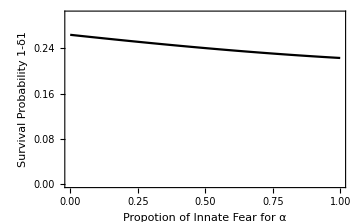

```mathematica
extreme1= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 10

```mathematica
λ=5;
di=0.3;
d1=0.4;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=10;
```

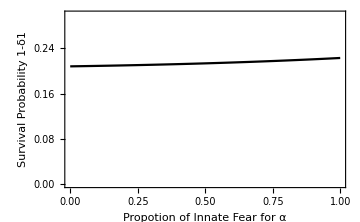

```mathematica
extreme2= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 15

```mathematica
λ=5;
di=0.3;
d1=0.4;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=15;
```

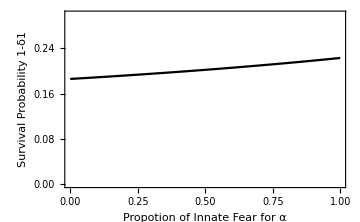

```mathematica
extreme3= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

### Medium Risk (Row 2)

#### Kf = 5

```mathematica
λ=5;
di=0.4;
d1=0.5;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=5;
```

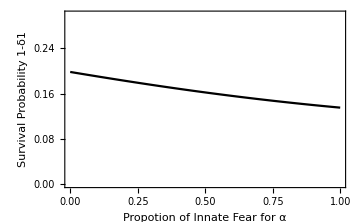

```mathematica
extreme4= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 10

```mathematica
λ=5;
di=0.4;
d1=0.5;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=10;
```

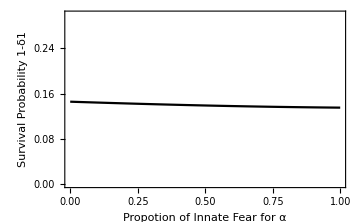

```mathematica
extreme5= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 15

```mathematica
λ=5;
di=0.4;
d1=0.5;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=15;
```

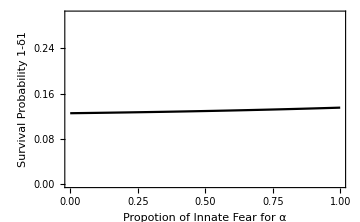

```mathematica
extreme6= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

### High Risk (Row 3)

#### Kf = 5

```mathematica
λ=5;
di=0.5;
d1=0.6;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=5;
```

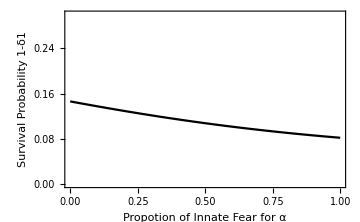

```mathematica
extreme7= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 10

```mathematica
λ=5;
di=0.5;
d1=0.6;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=10;
```

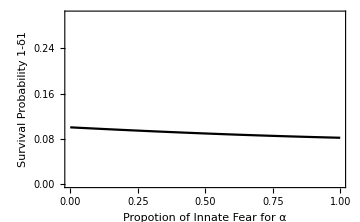

```mathematica
extreme8= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

#### Kf = 15

```mathematica
λ=5;
di=0.5;
d1=0.6;
α2 = .7; (*the value of this number doesn't change output*)
kd=5;
kf=15;
```

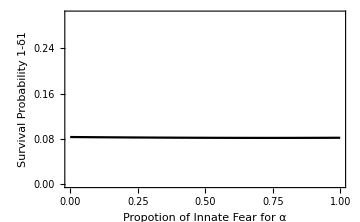

```mathematica
extreme9= Plot[1- DeltaOne[λ,di,d1,kd,kf,α1,α2],{α1,0,1},PlotRange->{0,.3}, PlotStyle->{Black}, FrameStyle->Directive[Thick,Black,12],Frame->{{True,False},{True,False}},ImageSize->Medium,
FrameLabel->{Text[Style["Propotion of Innate Fear for α",Black,12]],Text[Style["Survival Probability 1-δ1",Black,12]]}]
```

### Grid

```mathematica
extremegrid=Grid[{{Null,Text[Style["f  = 5",24,TextAlignment->Center]],Text[Style["Kf  = 10",24,TextAlignment->Center]],Text[Style["Kf TraditionalForm`=15",24,TextAlignment->Center]]},
{Rotate[Text[Style["low risk",24,TextAlignment->Center]],90 Degree],extreme1,extreme2,extreme3},
{Rotate[Text[Style["medium risk",24,TextAlignment->Center]],90Degree],extreme4,extreme5,extreme6},{Rotate[Text[Style["high risk",24,TextAlignment->Center]],90 Degree], extreme7,extreme8,extreme9}}]
```

| f  = 5 | Kf  = 10 | Kf TraditionalForm`=15
low risk | -Graphics- | -Graphics- | -Graphics-
medium risk | -Graphics- | -Graphics- | -Graphics-
high risk | -Graphics- | -Graphics- | -Graphics-

## Figure S2

```mathematica
(*note that function for this plot is included in the figure 2 code*)
```

### Row 1

#### Δ = .05

```mathematica
λ=10; (*parameters set*)
di=0.20;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2] (*run function*)
```

True

```mathematica
(*plot regions where learning fitness is indeed greater than innate fitness*)
```

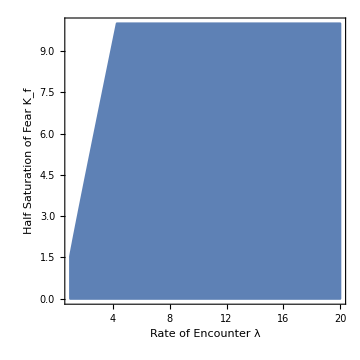

```mathematica
ntwrp10= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

```mathematica
.;,l
```

#### Δ = .1

```mathematica
λ=10;
di=0.15;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

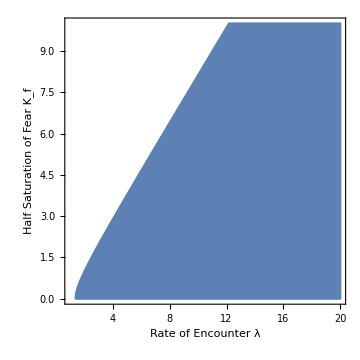

```mathematica
ntwrp11= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

#### Δ = .15

```mathematica
λ=10;
di=0.1;
d1=0.25;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

False

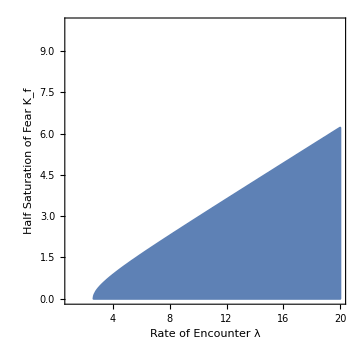

```mathematica
ntwrp12= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

```mathematica
Grid[{{ntwrp1,ntwrp2,ntwrp3}}]
```

ntwrp1 | ntwrp2 | ntwrp3

```mathematica
1. λ, kd - di = .15
```

### Row 2

#### Δ = .05

```mathematica
λ=10;
di=0.3;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

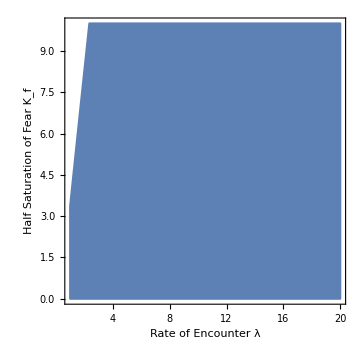

```mathematica
ntwrp13= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

#### Δ = .1

```mathematica
λ=10;
di=0.25;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

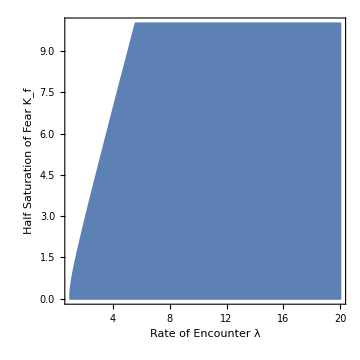

```mathematica
ntwrp14= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

#### Δ = .15

```mathematica
λ=10;
di=0.2;
d1=0.35;
kd=7;
kf=3;
α1=1;
α2=0;
TwoWins[λ,di,d1,kd,kf,α1,α2]
```

True

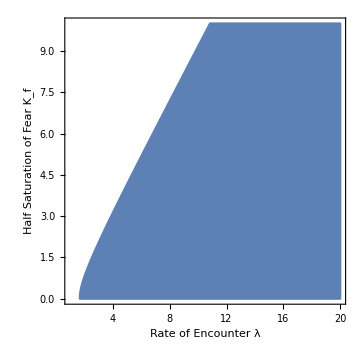

```mathematica
ntwrp15= Show[RegionPlot[TwoWins[λ,di,d1,kd,kf,α1,α2]==True,{λ,1,20},{kf,0,10}, ColorFunction->Blue],Axes->False,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Thick,Black,14],
FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},
ImageSize->Medium]
```

```mathematica
Grid[{{ntwrp4,ntwrp5,ntwrp6}}]
```

ntwrp4 | ntwrp5 | ntwrp6

```mathematica
Total Grid
```

Grid Total

```mathematica
twrpgrid=Grid[{{Null,Text[Style["TraditionalForm`Δ\ 0.05",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.1",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.15",26,TextAlignment->Center]]},
{Rotate[Text[Style["d0 = .25",26,TextAlignment->Center]],90 Degree],ntwrp1,ntwrp2,ntwrp3},
{Rotate[Text[Style["d0 = .35",26,TextAlignment->Center]],90Degree],ntwrp4,ntwrp5,ntwrp6}}]
```

| TraditionalForm`Δ\ 0.05 | TraditionalForm`Δ\ 0.1 | TraditionalForm`Δ\ 0.15
d0 = .25 | ntwrp1 | ntwrp2 | ntwrp3
d0 = .35 | ntwrp4 | ntwrp5 | ntwrp6

### Grid

```mathematica
twrpgrid2=Grid[{{Null,Text[Style["TraditionalForm`Δ\ 0.05",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.1",26,TextAlignment->Center]],Text[Style["TraditionalForm`Δ\ 0.15",26,TextAlignment->Center]]},
{Rotate[Text[Style["d0 = .25",26,TextAlignment->Center]],90 Degree],ntwrp10,ntwrp11,ntwrp12},
{Rotate[Text[Style["d0 = .35",26,TextAlignment->Center]],90Degree],ntwrp13,ntwrp14,ntwrp15}}]
```

| TraditionalForm`Δ\ 0.05 | TraditionalForm`Δ\ 0.1 | TraditionalForm`Δ\ 0.15
d0 = .25 | -Graphics- | -Graphics- | -Graphics-
d0 = .35 | -Graphics- | -Graphics- | -Graphics-

## Figure S3

### Data Points

```mathematica
(*data ran on cluster to expedite run time. Functions are copied below the data points for replication purposes*)
```

#### Δ = .02; Row 1

```mathematica
data = {{{0.1,0.1,0.},{0.1,0.2,0.6901524601711533},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,0.},{0.2,0.2,0.7473531022833539},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,0.},{0.30000000000000004,0.2,0.8071517897713685},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,0.},{0.4,0.2,0.8694527629724335},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.},{0.5,0.2,0.9341154736132635},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,0.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,0.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,0.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,0.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,0.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,0.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,0.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,0.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,0.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,0.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,0.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,0.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,0.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,0.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,0.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,0.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,0.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,0.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,0.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,0.9804096532139253}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,0.9769086635829868},{6.3,9.8,0.9180899466439768},{6.3,9.9,0.8717795671128383},{6.3,10.,0.8328264566491679}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,0.9861951421225842},{6.3999999999999995,9.5,0.9220211793543758},{6.3999999999999995,9.6,0.8726877421360281},{6.3999999999999995,9.700000000000001,0.8316536283417854},{6.3999999999999995,9.8,0.7961428439378551},{6.3999999999999995,9.9,0.7646620895177635},{6.3999999999999995,10.,0.7362955845583485}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,0.9365416001652646},{6.5,9.3,0.8818283359422944},{6.5,9.4,0.83734747198506},{6.5,9.5,0.7993475633763019},{6.5,9.6,0.7659442382674296},{6.5,9.700000000000001,0.7360282723868791},{6.5,9.8,0.7088792233831276},{6.5,9.9,0.6839967537115927},{6.5,10.,0.6610158838149571}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,0.9650782178780954},{6.6,9.,0.9008430527196547},{6.6,9.1,0.8508825951326776},{6.6,9.2,0.8091427344099799},{6.6,9.3,0.7729520724569665},{6.6,9.4,0.7408444347790376},{6.6,9.5,0.711909498707654},{6.6,9.6,0.6855341485505148},{6.6,9.700000000000001,0.6612818621877411},{6.6,9.8,0.6388275552940378},{6.6,9.9,0.6179215944293163},{6.6,10.,0.5983667839841214}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,0.9332961723800508},{6.7,8.8,0.8741814055799219},{6.7,8.9,0.8267459071453241},{6.7,9.,0.7865286061608938},{6.7,9.1,0.7513592210372835},{6.7,9.2,0.7199876134195035},{6.7,9.3,0.6916109676794148},{6.7,9.4,0.6656765527027633},{6.7,9.5,0.6417838142091086},{6.7,9.6,0.6196309569584729},{6.7,9.700000000000001,0.5989836026264893},{6.7,9.8,0.5796552079011977},{6.7,9.9,0.561494290522834},{6.7,10.,0.544375747637664}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,1.},{6.8,8.1,1.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,0.9883399854222625},{6.8,8.5,0.9111408693339448},{6.8,8.6,0.8543872324285628},{6.8,8.7,0.8081325998616364},{6.8,8.8,0.7686065059487653},{6.8,8.9,0.7338841108893628},{6.8,9.,0.7028211318445086},{6.8,9.1,0.6746692526296063},{6.8,9.2,0.6489061732426684},{6.8,9.3,0.6251497408333536},{6.8,9.4,0.6031095617202941},{6.8,9.5,0.5825587356985475},{6.8,9.6,0.563315762275558},{6.8,9.700000000000001,0.5452326122348885},{6.8,9.8,0.5281865961069018},{6.8,9.9,0.5120746250466797},{6.8,10.,0.4968090457766035}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,1.},{6.9,7.9,1.},{6.9,8.,1.},{6.9,8.1,1.},{6.9,8.2,0.9715162759369828},{6.9,8.3,0.8964952734845459},{6.9,8.4,0.8403634323076273},{6.9,8.5,0.794315198119083},{6.9,8.6,0.7548381387742255},{6.9,8.7,0.7200971243336435},{6.9,8.8,0.6889856881660912},{6.9,8.9,0.6607738070766787},{6.9,9.,0.6349485527906714},{6.9,9.1,0.6111323728287007},{6.9,9.2,0.5890375349896355},{6.9,9.3,0.5684384320319267},{6.9,9.4,0.5491541076419505},{6.9,9.5,0.5310366672151394},{6.9,9.6,0.5139633158270803},{6.9,9.700000000000001,0.49783071555688846},{6.9,9.8,0.4825508886953072},{6.9,9.9,0.46804818103983264},{6.9,10.,0.4542569395970564}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,1.},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,1.},{7.,5.2,1.},{7.,5.3,1.},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,1.},{7.,7.7,1.},{7.,7.8,1.},{7.,7.9,1.},{7.,8.,0.9643780937947475},{7.,8.1,0.8884478660881622},{7.,8.2,0.8315687020130658},{7.,8.3,0.784906700706036},{7.,8.4,0.7449167849192498},{7.,8.5,0.7097410388935115},{7.,8.6,0.6782577282755957},{7.,8.7,0.6497250676381762},{7.,8.8,0.6236217008220515},{7.,8.9,0.5995637126334232},{7.,9.,0.5772579546500181},{7.,9.1,0.5564749098738058},{7.,9.2,0.5370300837104381},{7.,9.3,0.518772811360825},{7.,9.4,0.501577897852712},{7.,9.5,0.48533998016072005},{7.,9.6,0.4699693505386486},{7.,9.700000000000001,0.45538884678966113},{7.,9.8,0.4415315266323501},{7.,9.9,0.4283388699054297},{7.,10.,0.41575926119204953}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,1.},{7.1,4.8,1.},{7.1,4.9,1.},{7.1,5.,1.},{7.1,5.1,1.},{7.1,5.2,1.},{7.1,5.3,1.},{7.1,5.4,1.},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,1.},{7.1,7.5,1.},{7.1,7.6,1.},{7.1,7.7,1.},{7.1,7.8,0.966492109651794},{7.1,7.9,0.8867629100656539},{7.1,8.,0.8278239849393116},{7.1,8.1,0.7797547915304932},{7.1,8.2,0.7387057463027784},{7.1,8.3,0.7026900836144115},{7.1,8.4,0.6705184716380124},{7.1,8.5,0.6414098606145605},{7.1,8.6,0.614817198964687},{7.1,8.7,0.5903389149201548},{7.1,8.8,0.5676694482417545},{7.1,8.9,0.5465695871067181},{7.1,9.,0.5268477007054048},{7.1,9.1,0.5083473659156926},{7.1,9.2,0.49093872124309973},{7.1,9.3,0.4745127258539734},{7.1,9.4,0.45897694780006093},{7.1,9.5,0.4442503307498483},{7.1,9.6,0.4302649965984773},{7.1,9.700000000000001,0.41696008260806205},{7.1,9.8,0.4042823965999786},{7.1,9.9,0.3921848357159548},{7.1,10.,0.3806256267188326}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,1.},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,1.},{7.199999999999999,4.7,1.},{7.199999999999999,4.8,1.},{7.199999999999999,4.9,1.},{7.199999999999999,5.,1.},{7.199999999999999,5.1,1.},{7.199999999999999,5.2,1.},{7.199999999999999,5.3,1.},{7.199999999999999,5.4,1.},{7.199999999999999,5.5,1.},{7.199999999999999,5.6,1.},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,1.},{7.199999999999999,7.4,1.},{7.199999999999999,7.5,1.},{7.199999999999999,7.6,0.9789840262340324},{7.199999999999999,7.7,0.8917501847322808},{7.199999999999999,7.8,0.8292516545099085},{7.199999999999999,7.9,0.7789054482040197},{7.199999999999999,8.,0.7362124091253268},{7.199999999999999,8.1,0.6989285967102405},{7.199999999999999,8.2,0.665738423871861},{7.199999999999999,8.3,0.6357892234617474},{7.199999999999999,8.4,0.6084894369783503},{7.199999999999999,8.5,0.5834078898525694},{7.199999999999999,8.6,0.5602182839043974},{7.199999999999999,8.7,0.5386662983835471},{7.199999999999999,8.8,0.5185488611913219},{7.199999999999999,8.9,0.4997008374798402},{7.199999999999999,9.,0.4819849010698407},{7.199999999999999,9.1,0.4652879488815502},{7.199999999999999,9.2,0.44951092630747114},{7.199999999999999,9.3,0.4345709073264353},{7.199999999999999,9.4,0.4203955587436898},{7.199999999999999,9.5,0.4069216701045606},{7.199999999999999,9.6,0.3940938714497892},{7.199999999999999,9.700000000000001,0.3818630784460742},{7.199999999999999,9.8,0.370185662374169},{7.199999999999999,9.9,0.3590226188225873},{7.199999999999999,10.,0.3483389125730418}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,1.},{7.3,3.1,1.},{7.3,3.2,1.},{7.3,3.3000000000000003,1.},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,1.},{7.3,4.6,1.},{7.3,4.7,1.},{7.3,4.8,1.},{7.3,4.9,1.},{7.3,5.,1.},{7.3,5.1,1.},{7.3,5.2,1.},{7.3,5.3,1.},{7.3,5.4,1.},{7.3,5.5,1.},{7.3,5.6,1.},{7.3,5.7,1.},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,1.},{7.3,7.2,1.},{7.3,7.3,1.},{7.3,7.4,1.},{7.3,7.5,0.9043632697846069},{7.3,7.6,0.836289125315998},{7.3,7.7,0.7826037869133168},{7.3,7.8,0.7375843669873706},{7.3,7.9,0.6985477871687478},{7.3,8.,0.6639724790790071},{7.3,8.1,0.6328933796009333},{7.3,8.2,0.6046510588133654},{7.3,8.3,0.5787702258022484},{7.3,8.4,0.5548942911499432},{7.3,8.5,0.5327472210478507},{7.3,8.6,0.5121099468450091},{7.3,8.7,0.4928048443100409},{7.3,8.8,0.4746857203504378},{7.3,8.9,0.4576302000475927},{7.3,9.,0.44153474516740093},{7.3,9.1,0.4263107228250583},{7.3,9.2,0.411881608401871},{7.3,9.3,0.398180739207875},{7.3,9.4,0.3851497134501683},{7.3,9.5,0.37273682615792575},{7.3,9.6,0.3608963760302361},{7.3,9.700000000000001,0.3495873063662259},{7.3,9.8,0.33877303202717657},{7.3,9.9,0.32842044280308486},{7.3,10.,0.3184995580784499}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,1.},{7.3999999999999995,3.0000000000000004,1.},{7.3999999999999995,3.1,1.},{7.3999999999999995,3.2,1.},{7.3999999999999995,3.3000000000000003,1.},{7.3999999999999995,3.4000000000000004,1.},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,1.},{7.3999999999999995,4.5,1.},{7.3999999999999995,4.6,1.},{7.3999999999999995,4.7,1.},{7.3999999999999995,4.8,1.},{7.3999999999999995,4.9,1.},{7.3999999999999995,5.,1.},{7.3999999999999995,5.1,1.},{7.3999999999999995,5.2,1.},{7.3999999999999995,5.3,1.},{7.3999999999999995,5.4,1.},{7.3999999999999995,5.5,1.},{7.3999999999999995,5.6,1.},{7.3999999999999995,5.7,1.},{7.3999999999999995,5.8,1.},{7.3999999999999995,5.9,1.},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,1.},{7.3999999999999995,7.,1.},{7.3999999999999995,7.1,1.},{7.3999999999999995,7.2,1.},{7.3999999999999995,7.3,0.9266287797733599},{7.3999999999999995,7.4,0.8498075220378337},{7.3999999999999995,7.5,0.7913358428712813},{7.3999999999999995,7.6,0.7431283174298997},{7.3999999999999995,7.7,0.7017538688687679},{7.3999999999999995,7.8,0.6653639699899419},{7.3999999999999995,7.9,0.632823421542965},{7.3999999999999995,8.,0.6033732268619938},{7.3999999999999995,8.1,0.5764750509639768},{7.3999999999999995,8.2,0.551729848468476},{7.3999999999999995,8.3,0.52883184376696},{7.3999999999999995,8.4,0.5075399691145908},{7.3999999999999995,8.5,0.48766031468656607},{7.3999999999999995,8.6,0.4690338929119275},{7.3999999999999995,8.7,0.4515284224485543},{7.3999999999999995,8.8,0.4350321909544959},{7.3999999999999995,8.9,0.4194502051808643},{7.3999999999999995,9.,0.4047004960853179},{7.3999999999999995,9.1,0.3907119309548141},{7.3999999999999995,9.2,0.3774222668157948},{7.3999999999999995,9.3,0.36477664799672144},{7.3999999999999995,9.4,0.3527265626811698},{7.3999999999999995,9.5,0.3412286321275205},{7.3999999999999995,9.6,0.3302441126763639},{7.3999999999999995,9.700000000000001,0.31973813050174377},{7.3999999999999995,9.8,0.3096791946623729},{7.3999999999999995,9.9,0.30003949259528584},{7.3999999999999995,10.,0.29079083692560276}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,1.},{7.5,3.0000000000000004,1.},{7.5,3.1,1.},{7.5,3.2,1.},{7.5,3.3000000000000003,1.},{7.5,3.4000000000000004,1.},{7.5,3.5000000000000004,1.},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,1.},{7.5,4.3999999999999995,1.},{7.5,4.5,1.},{7.5,4.6,1.},{7.5,4.7,1.},{7.5,4.8,1.},{7.5,4.9,1.},{7.5,5.,1.},{7.5,5.1,1.},{7.5,5.2,1.},{7.5,5.3,1.},{7.5,5.4,1.},{7.5,5.5,1.},{7.5,5.6,1.},{7.5,5.7,1.},{7.5,5.8,1.},{7.5,5.9,1.},{7.5,6.,1.},{7.5,6.1,1.},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,1.},{7.5,6.9,1.},{7.5,7.,1.},{7.5,7.1,0.9630726320316935},{7.5,7.2,0.8713810275997471},{7.5,7.3,0.8059272716884394},{7.5,7.4,0.7533555563183815},{7.5,7.5,0.708892018145236},{7.5,7.6,0.6701584345667674},{7.5,7.7,0.6357595418907992},{7.5,7.8,0.6047906881407689},{7.5,7.9,0.5766240674249716},{7.5,8.,0.550801999555711},{7.5,8.1,0.5269778242873141},{7.5,8.2,0.5048816412178082},{7.5,8.3,0.4842979129149512},{7.5,8.4,0.4650505096393967},{7.5,8.5,0.4469948599415474},{7.5,8.6,0.4300089358010896},{7.5,8.7,0.41398938394799173},{7.5,8.8,0.39884747223605915},{7.5,8.9,0.38450640150617243},{7.5,9.,0.3708992668589634},{7.5,9.1,0.3579673478621064},{7.5,9.2,0.34565848157437085},{7.5,9.3,0.33392658293251914},{7.5,9.4,0.32273032906490345},{7.5,9.5,0.312032653617756},{7.5,9.6,0.30179979456598555},{7.5,9.700000000000001,0.29200252581575187},{7.5,9.8,0.282612376243185},{7.5,9.9,0.27360466552689117},{7.5,10.,0.2649565201716404}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,1.},{7.6,2.9000000000000004,1.},{7.6,3.0000000000000004,1.},{7.6,3.1,1.},{7.6,3.2,1.},{7.6,3.3000000000000003,1.},{7.6,3.4000000000000004,1.},{7.6,3.5000000000000004,1.},{7.6,3.6,1.},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,1.},{7.6,4.3,1.},{7.6,4.3999999999999995,1.},{7.6,4.5,1.},{7.6,4.6,1.},{7.6,4.7,1.},{7.6,4.8,1.},{7.6,4.9,1.},{7.6,5.,1.},{7.6,5.1,1.},{7.6,5.2,1.},{7.6,5.3,1.},{7.6,5.4,1.},{7.6,5.5,1.},{7.6,5.6,1.},{7.6,5.7,1.},{7.6,5.8,1.},{7.6,5.9,1.},{7.6,6.,1.},{7.6,6.1,1.},{7.6,6.2,1.},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,1.},{7.6,6.7,1.},{7.6,6.8,1.},{7.6,6.9,1.},{7.6,7.,0.9040302413856077},{7.6,7.1,0.8277599755324648},{7.6,7.2,0.7690728257480487},{7.6,7.3,0.7204933274230669},{7.6,7.4,0.6787303619318087},{7.6,7.5,0.6419775456674858},{7.6,7.6,0.6091124542606766},{7.6,7.7,0.5793786746893986},{7.6,7.8,0.5522366077966078},{7.6,7.9,0.5272844302376307},{7.6,8.,0.5042130306871548},{7.6,8.1,0.4827770832041175},{7.6,8.2,0.46278339984710415},{7.6,8.3,0.44406640526811103},{7.6,8.4,0.42649260281856305},{7.6,8.5,0.40994804184766126},{7.6,8.6,0.3943356702060579},{7.6,8.7,0.37957184125457993},{7.6,8.8,0.3655837013770089},{7.6,8.9,0.35230760378681036},{7.6,9.,0.33968744462062395},{7.6,9.1,0.32767342683313794},{7.6,9.2,0.3162212889396218},{7.6,9.3,0.30529121125566455},{7.6,9.4,0.2948475731872465},{7.6,9.5,0.2848580840842397},{7.6,9.6,0.2752935453460737},{7.6,9.700000000000001,0.26612726946174436},{7.6,9.8,0.25733502027439914},{7.6,9.9,0.2488946282431435},{7.6,10.,0.24078574672139313}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,1.},{7.7,2.8000000000000003,1.},{7.7,2.9000000000000004,1.},{7.7,3.0000000000000004,1.},{7.7,3.1,1.},{7.7,3.2,1.},{7.7,3.3000000000000003,1.},{7.7,3.4000000000000004,1.},{7.7,3.5000000000000004,1.},{7.7,3.6,1.},{7.7,3.7,1.},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,1.},{7.7,4.2,1.},{7.7,4.3,1.},{7.7,4.3999999999999995,1.},{7.7,4.5,1.},{7.7,4.6,1.},{7.7,4.7,1.},{7.7,4.8,1.},{7.7,4.9,1.},{7.7,5.,1.},{7.7,5.1,1.},{7.7,5.2,1.},{7.7,5.3,1.},{7.7,5.4,1.},{7.7,5.5,1.},{7.7,5.6,1.},{7.7,5.7,1.},{7.7,5.8,1.},{7.7,5.9,1.},{7.7,6.,1.},{7.7,6.1,1.},{7.7,6.2,1.},{7.7,6.3,1.},{7.7,6.4,1.},{7.7,6.5,1.},{7.7,6.6,1.},{7.7,6.7,1.},{7.7,6.8,0.9547513073383269},{7.7,6.9,0.8592839522767459},{7.7,7.,0.7915679946532743},{7.7,7.1,0.7373617263105134},{7.7,7.2,0.6916307255823517},{7.7,7.3,0.6518773962160108},{7.7,7.4,0.6166401865678276},{7.7,7.5,0.5849724537685943},{7.7,7.6,0.5562180086978696},{7.7,7.7,0.5298986069159067},{7.7,7.8,0.5056524838383419},{7.7,7.9,0.48319648124284437},{7.7,8.,0.46231029047271516},{7.7,8.1,0.4428058814149523},{7.7,8.2,0.42453363290844637},{7.7,8.3,0.4073666081267296},{7.7,8.4,0.3911971465434193},{7.7,8.5,0.3759328221389887},{7.7,8.6,0.361493851960447},{7.7,8.7,0.3478105323709954},{7.7,8.8,0.33482175861056085},{7.7,8.9,0.32247350564944205},{7.7,9.,0.31071772400178066},{7.7,9.1,0.2995127708342853},{7.7,9.2,0.2888166147983094},{7.7,9.3,0.27859815059238335},{7.7,9.4,0.2688248473095528},{7.7,9.5,0.2594682299489302},{7.7,9.6,0.25050245680296307},{7.7,9.700000000000001,0.2419038415623073},{7.7,9.8,0.2336505804564355},{7.7,9.9,0.22572291874296535},{7.7,10.,0.2181024809776143}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,1.},{7.8,2.8000000000000003,1.},{7.8,2.9000000000000004,1.},{7.8,3.0000000000000004,1.},{7.8,3.1,1.},{7.8,3.2,1.},{7.8,3.3000000000000003,1.},{7.8,3.4000000000000004,1.},{7.8,3.5000000000000004,1.},{7.8,3.6,1.},{7.8,3.7,1.},{7.8,3.8000000000000003,1.},{7.8,3.9000000000000004,1.},{7.8,4.,1.},{7.8,4.1,1.},{7.8,4.2,1.},{7.8,4.3,1.},{7.8,4.3999999999999995,1.},{7.8,4.5,1.},{7.8,4.6,1.},{7.8,4.7,1.},{7.8,4.8,1.},{7.8,4.9,1.},{7.8,5.,1.},{7.8,5.1,1.},{7.8,5.2,1.},{7.8,5.3,1.},{7.8,5.4,1.},{7.8,5.5,1.},{7.8,5.6,1.},{7.8,5.7,1.},{7.8,5.8,1.},{7.8,5.9,1.},{7.8,6.,1.},{7.8,6.1,1.},{7.8,6.2,1.},{7.8,6.3,1.},{7.8,6.4,1.},{7.8,6.5,1.},{7.8,6.6,1.},{7.8,6.7,0.9055121777308867},{7.8,6.8,0.8230209348524186},{7.8,6.9,0.7607418625043865},{7.8,7.,0.7096713070980875},{7.8,7.1,0.6660316270517748},{7.8,7.2,0.6277981963206013},{7.8,7.3,0.5937308325598054},{7.8,7.4,0.5630019297067401},{7.8,7.5,0.5350251480158882},{7.8,7.6,0.50936618166165},{7.8,7.7,0.48569275106788645},{7.8,7.8,0.463742635472902},{7.8,7.9,0.44330535822406025},{7.8,8.,0.424208347986937},{7.8,8.1,0.4063080774808707},{7.8,8.2,0.3894836087377203},{7.8,8.3,0.37363189917281947},{7.8,8.4,0.35866428822522406},{7.8,8.5,0.3445038439863825},{7.8,8.6,0.3310833175600425},{7.8,8.7,0.318343510555852},{7.8,8.8,0.30623194767839007},{7.8,8.9,0.29470215144233813},{7.8,9.,0.28371222555960496},{7.8,9.1,0.2732246783037313},{7.8,9.2,0.2632057073153803},{7.8,9.3,0.25362462720296947},{7.8,9.4,0.24445365492350296},{7.8,9.5,0.23566738466887438},{7.8,9.6,0.22724261397367418},{7.8,9.700000000000001,0.21915807371956436},{7.8,9.8,0.2113942151397603},{7.8,9.9,0.20393303860614098},{7.8,10.,0.19675791318363575}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,1.},{7.9,2.7,1.},{7.9,2.8000000000000003,1.},{7.9,2.9000000000000004,1.},{7.9,3.0000000000000004,1.},{7.9,3.1,1.},{7.9,3.2,1.},{7.9,3.3000000000000003,1.},{7.9,3.4000000000000004,1.},{7.9,3.5000000000000004,1.},{7.9,3.6,1.},{7.9,3.7,1.},{7.9,3.8000000000000003,1.},{7.9,3.9000000000000004,1.},{7.9,4.,1.},{7.9,4.1,1.},{7.9,4.2,1.},{7.9,4.3,1.},{7.9,4.3999999999999995,1.},{7.9,4.5,1.},{7.9,4.6,1.},{7.9,4.7,1.},{7.9,4.8,1.},{7.9,4.9,1.},{7.9,5.,1.},{7.9,5.1,1.},{7.9,5.2,1.},{7.9,5.3,1.},{7.9,5.4,1.},{7.9,5.5,1.},{7.9,5.6,1.},{7.9,5.7,1.},{7.9,5.8,1.},{7.9,5.9,1.},{7.9,6.,1.},{7.9,6.1,1.},{7.9,6.2,1.},{7.9,6.3,1.},{7.9,6.4,1.},{7.9,6.5,0.9807917815092496},{7.9,6.6,0.8676004275107152},{7.9,6.7,0.7926794935306921},{7.9,6.8,0.7340856269511788},{7.9,6.9,0.6852699020271155},{7.9,7.,0.6431834382600877},{7.9,7.1,0.6061030828327565},{7.9,7.2,0.5729372127164675},{7.9,7.3,0.5429410287905632},{7.9,7.4,0.5155778330066665},{7.9,7.5,0.4904451588537112},{7.9,7.6,0.4672318370005897},{7.9,7.7,0.44569080899359576},{7.9,7.8,0.4256220390766779},{7.9,7.9,0.40686080786505957},{7.9,8.,0.38926946090289366},{7.9,8.1,0.37273143599798986},{7.9,8.2,0.35714726991531376},{7.9,8.3,0.34243112895795363},{7.9,8.4,0.3285083590788114},{7.9,8.5,0.31531332758641756},{7.9,8.6,0.3027872447873618},{7.9,8.7,0.29088231057692693},{7.9,8.8,0.2795494799261555},{7.9,8.9,0.2687489942535637},{7.9,9.,0.25844407200303776},{7.9,9.1,0.2486015191351381},{7.9,9.2,0.2391911412165031},{7.9,9.3,0.2301856275043835},{7.9,9.4,0.22155997013938641},{7.9,9.5,0.21329132306832432},{7.9,9.6,0.2053587186796848},{7.9,9.700000000000001,0.19774288150030414},{7.9,9.8,0.19042601631339431},{7.9,9.9,0.18339180311721548},{7.9,10.,0.17662496763483398}},{{8.,0.1,1.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,1.},{8.,2.4000000000000004,1.},{8.,2.5000000000000004,1.},{8.,2.6,1.},{8.,2.7,1.},{8.,2.8000000000000003,1.},{8.,2.9000000000000004,1.},{8.,3.0000000000000004,1.},{8.,3.1,1.},{8.,3.2,1.},{8.,3.3000000000000003,1.},{8.,3.4000000000000004,1.},{8.,3.5000000000000004,1.},{8.,3.6,1.},{8.,3.7,1.},{8.,3.8000000000000003,1.},{8.,3.9000000000000004,1.},{8.,4.,1.},{8.,4.1,1.},{8.,4.2,1.},{8.,4.3,1.},{8.,4.3999999999999995,1.},{8.,4.5,1.},{8.,4.6,1.},{8.,4.7,1.},{8.,4.8,1.},{8.,4.9,1.},{8.,5.,1.},{8.,5.1,1.},{8.,5.2,1.},{8.,5.3,1.},{8.,5.4,1.},{8.,5.5,1.},{8.,5.6,1.},{8.,5.7,1.},{8.,5.8,1.},{8.,5.9,1.},{8.,6.,1.},{8.,6.1,1.},{8.,6.2,1.},{8.,6.3,1.},{8.,6.4,0.9355891020181963},{8.,6.5,0.8369326187939268},{8.,6.6,0.7668624696207698},{8.,6.7,0.7108365269801202},{8.,6.8,0.6636519027563244},{8.,6.9,0.6227141424430828},{8.,7.,0.5864993932259261},{8.,7.1,0.5540187551898034},{8.,7.2,0.5245854297342692},{8.,7.3,0.4976984021224691},{8.,7.4,0.4729781188009742},{8.,7.5,0.45012895144890114},{8.,7.6,0.42891453066291974},{8.,7.7,0.4091426669424769},{8.,7.8,0.390654318065001},{8.,7.9,0.3733161470493192},{8.,8.,0.3570150494134002},{8.,8.1,0.34165388616664266},{8.,8.2,0.3271489343189837},{8.,8.3,0.3134270379244822},{8.,8.4,0.30042459470964916},{8.,8.5,0.2880832530438196},{8.,8.6,0.2763543950142267},{8.,8.7,0.2651924643932822},{8.,8.8,0.25455722899131705},{8.,8.9,0.24441247161628504},{8.,9.,0.2347253469662469},{8.,9.1,0.22546609385908498},{8.,9.2,0.21660769972586},{8.,9.3,0.20812544568942792},{8.,9.4,0.19999672347706376},{8.,9.5,0.1922007943778461},{8.,9.6,0.18471856365104294},{8.,9.700000000000001,0.17753243901513757},{8.,9.8,0.17062616419727025},{8.,9.9,0.16398468966317892},{8.,10.,0.15759405607988947}},{{8.1,0.1,1.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,1.},{8.1,1.8000000000000003,1.},{8.1,1.9000000000000001,1.},{8.1,2.,1.},{8.1,2.1,1.},{8.1,2.2,1.},{8.1,2.3000000000000003,1.},{8.1,2.4000000000000004,1.},{8.1,2.5000000000000004,1.},{8.1,2.6,1.},{8.1,2.7,1.},{8.1,2.8000000000000003,1.},{8.1,2.9000000000000004,1.},{8.1,3.0000000000000004,1.},{8.1,3.1,1.},{8.1,3.2,1.},{8.1,3.3000000000000003,1.},{8.1,3.4000000000000004,1.},{8.1,3.5000000000000004,1.},{8.1,3.6,1.},{8.1,3.7,1.},{8.1,3.8000000000000003,1.},{8.1,3.9000000000000004,1.},{8.1,4.,1.},{8.1,4.1,1.},{8.1,4.2,1.},{8.1,4.3,1.},{8.1,4.3999999999999995,1.},{8.1,4.5,1.},{8.1,4.6,1.},{8.1,4.7,1.},{8.1,4.8,1.},{8.1,4.9,1.},{8.1,5.,1.},{8.1,5.1,1.},{8.1,5.2,1.},{8.1,5.3,1.},{8.1,5.4,1.},{8.1,5.5,1.},{8.1,5.6,1.},{8.1,5.7,1.},{8.1,5.8,1.},{8.1,5.9,1.},{8.1,6.,1.},{8.1,6.1,1.},{8.1,6.2,1.},{8.1,6.3,0.9020694458769583},{8.1,6.4,0.8115658746888037},{8.1,6.5,0.7447146285291877},{8.1,6.6,0.6904766789889758},{8.1,6.7,0.6444538049664204},{8.1,6.8,0.6043453727454388},{8.1,6.9,0.5687624832126246},{8.1,7.,0.5367869344087124},{8.1,7.1,0.507772671814031},{8.1,7.2,0.4812437897070951},{8.1,7.3,0.45683706168133337},{8.1,7.4,0.4342676925425657},{8.1,7.5,0.41330707515093035},{8.1,7.6,0.39376859289994703},{8.1,7.7,0.3754971009241315},{8.1,7.8,0.358362343508269},{8.1,7.9,0.3422533161289898},{8.1,8.,0.3270749346155076},{8.1,8.1,0.31274460107182744},{8.1,8.2,0.299192042123933},{8.1,8.3,0.2863490811775904},{8.1,8.4,0.2741645344263297},{8.1,8.5,0.26258707916310403},{8.1,8.6,0.2515722370069607},{8.1,8.7,0.24108026370711866},{8.1,8.8,0.23107501014522697},{8.1,8.9,0.22152411404441677},{8.1,9.,0.21239804115997576},{8.1,9.1,0.20366993939731462},{8.1,9.2,0.19531527405963856},{8.1,9.3,0.18731159862205962},{8.1,9.4,0.17963828809210317},{8.1,9.5,0.17227642853847988},{8.1,9.6,0.16520847151151943},{8.1,9.700000000000001,0.15841827709105588},{8.1,9.8,0.1518908800635921},{8.1,9.9,0.14561233649240168},{8.1,10.,0.1395699340258113}},{{8.2,0.1,1.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,1.},{8.2,1.8000000000000003,1.},{8.2,1.9000000000000001,1.},{8.2,2.,1.},{8.2,2.1,1.},{8.2,2.2,1.},{8.2,2.3000000000000003,1.},{8.2,2.4000000000000004,1.},{8.2,2.5000000000000004,1.},{8.2,2.6,1.},{8.2,2.7,1.},{8.2,2.8000000000000003,1.},{8.2,2.9000000000000004,1.},{8.2,3.0000000000000004,1.},{8.2,3.1,1.},{8.2,3.2,1.},{8.2,3.3000000000000003,1.},{8.2,3.4000000000000004,1.},{8.2,3.5000000000000004,1.},{8.2,3.6,1.},{8.2,3.7,1.},{8.2,3.8000000000000003,1.},{8.2,3.9000000000000004,1.},{8.2,4.,1.},{8.2,4.1,1.},{8.2,4.2,1.},{8.2,4.3,1.},{8.2,4.3999999999999995,1.},{8.2,4.5,1.},{8.2,4.6,1.},{8.2,4.7,1.},{8.2,4.8,1.},{8.2,4.9,1.},{8.2,5.,1.},{8.2,5.1,1.},{8.2,5.2,1.},{8.2,5.3,1.},{8.2,5.4,1.},{8.2,5.5,1.},{8.2,5.6,1.},{8.2,5.7,1.},{8.2,5.8,1.},{8.2,5.9,1.},{8.2,6.,1.},{8.2,6.1,1.},{8.2,6.2,0.8759647367203705},{8.2,6.3,0.7904063462463217},{8.2,6.4,0.725674380195423},{8.2,6.5,0.6726406387370111},{8.2,6.6,0.627407071451082},{8.2,6.7,0.5878656326385533},{8.2,6.8,0.5527173883363967},{8.2,6.9,0.5210922308180291},{8.2,7.,0.4923718366327228},{8.2,7.1,0.4660971787372276},{8.2,7.2,0.4419161912607833},{8.2,7.3,0.419551381265882},{8.2,7.4,0.39877926382753226},{8.2,7.5,0.3794166760842544},{8.2,7.6,0.3613112097584006},{8.2,7.7,0.34433448705445363},{8.2,7.8,0.32837687296329093},{8.2,7.9,0.3133444162486148},{8.2,8.,0.2991570252007913},{8.2,8.1,0.28573840102979114},{8.2,8.2,0.27303067918332036},{8.2,8.3,0.260976658242869},{8.2,8.4,0.24952689278886908},{8.2,8.5,0.23863721280094358},{8.2,8.6,0.22826792575809512},{8.2,8.7,0.21838327320049336},{8.2,8.8,0.20895087399154155},{8.2,8.9,0.1999413238477266},{8.2,9.,0.1913279012192493},{8.2,9.1,0.18308627434733415},{8.2,9.2,0.17519381907052228},{8.2,9.3,0.16763021814645},{8.2,9.4,0.16037637306342545},{8.2,9.5,0.1534149968723642},{8.2,9.6,0.1467298667077311},{8.2,9.700000000000001,0.1403060870483334},{8.2,9.8,0.13412981374538982},{8.2,9.9,0.1281881841112709},{8.2,10.,0.1224692147647173}},{{8.3,0.1,1.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,1.},{8.3,1.7000000000000002,1.},{8.3,1.8000000000000003,1.},{8.3,1.9000000000000001,1.},{8.3,2.,1.},{8.3,2.1,1.},{8.3,2.2,1.},{8.3,2.3000000000000003,1.},{8.3,2.4000000000000004,1.},{8.3,2.5000000000000004,1.},{8.3,2.6,1.},{8.3,2.7,1.},{8.3,2.8000000000000003,1.},{8.3,2.9000000000000004,1.},{8.3,3.0000000000000004,1.},{8.3,3.1,1.},{8.3,3.2,1.},{8.3,3.3000000000000003,1.},{8.3,3.4000000000000004,1.},{8.3,3.5000000000000004,1.},{8.3,3.6,1.},{8.3,3.7,1.},{8.3,3.8000000000000003,1.},{8.3,3.9000000000000004,1.},{8.3,4.,1.},{8.3,4.1,1.},{8.3,4.2,1.},{8.3,4.3,1.},{8.3,4.3999999999999995,1.},{8.3,4.5,1.},{8.3,4.6,1.},{8.3,4.7,1.},{8.3,4.8,1.},{8.3,4.9,1.},{8.3,5.,1.},{8.3,5.1,1.},{8.3,5.2,1.},{8.3,5.3,1.},{8.3,5.4,1.},{8.3,5.5,1.},{8.3,5.6,1.},{8.3,5.7,1.},{8.3,5.8,1.},{8.3,5.9,1.},{8.3,6.,0.9877739890735374},{8.3,6.1,0.8553576120712205},{8.3,6.2,0.7727798960701859},{8.3,6.3,0.7093579975519962},{8.3,6.4,0.657064204308473},{8.3,6.5,0.6123107774701398},{8.3,6.6,0.5731119683124961},{8.3,6.7,0.5382267079053009},{8.3,6.8,0.5068152950399937},{8.3,6.9,0.47827686692327853},{8.3,7.,0.4521629686187334},{8.3,7.1,0.4281282055799459},{8.3,7.2,0.4058994039615328},{8.3,7.3,0.3852558685014001},{8.3,7.4,0.36601658030219864},{8.3,7.5,0.3480302862867742},{8.3,7.6,0.3311696677276667},{8.3,7.7,0.3153258818598983},{8.3,7.8,0.3004058756703324},{8.3,7.9,0.28632646481338503},{8.3,8.,0.2730183661964669},{8.3,8.1,0.2604182661249287},{8.3,8.2,0.24847087383449815},{8.3,8.3,0.23712676441947395},{8.3,8.4,0.2263417251022186},{8.3,8.5,0.21607617537981394},{8.3,8.6,0.20629436560651906},{8.3,8.7,0.1969639308498659},{8.3,8.8,0.18805549656237486},{8.3,8.9,0.17954228136079878},{8.3,9.,0.1713999073788696},{8.3,9.1,0.16360590283842355},{8.3,9.2,0.15613978707745785},{8.3,9.3,0.1489825894542165},{8.3,9.4,0.1421168786930379},{8.3,9.5,0.1355265064013055},{8.3,9.6,0.12919661553534967},{8.3,9.700000000000001,0.12311325052120861},{8.3,9.8,0.11726365325687055},{8.3,9.9,0.11163575740020455},{8.3,10.,0.10621842369316348}},{{8.4,0.1,1.},{8.4,0.2,1.},{8.4,0.30000000000000004,1.},{8.4,0.4,1.},{8.4,0.5,1.},{8.4,0.6,1.},{8.4,0.7000000000000001,1.},{8.4,0.8,1.},{8.4,0.9,1.},{8.4,1.,1.},{8.4,1.1,1.},{8.4,1.2000000000000002,1.},{8.4,1.3000000000000003,1.},{8.4,1.4000000000000001,1.},{8.4,1.5000000000000002,1.},{8.4,1.6,1.},{8.4,1.7000000000000002,1.},{8.4,1.8000000000000003,1.},{8.4,1.9000000000000001,1.},{8.4,2.,1.},{8.4,2.1,1.},{8.4,2.2,1.},{8.4,2.3000000000000003,1.},{8.4,2.4000000000000004,1.},{8.4,2.5000000000000004,1.},{8.4,2.6,1.},{8.4,2.7,1.},{8.4,2.8000000000000003,1.},{8.4,2.9000000000000004,1.},{8.4,3.0000000000000004,1.},{8.4,3.1,1.},{8.4,3.2,1.},{8.4,3.3000000000000003,1.},{8.4,3.4000000000000004,1.},{8.4,3.5000000000000004,1.},{8.4,3.6,1.},{8.4,3.7,1.},{8.4,3.8000000000000003,1.},{8.4,3.9000000000000004,1.},{8.4,4.,1.},{8.4,4.1,1.},{8.4,4.2,1.},{8.4,4.3,1.},{8.4,4.3999999999999995,1.},{8.4,4.5,1.},{8.4,4.6,1.},{8.4,4.7,1.},{8.4,4.8,1.},{8.4,4.9,1.},{8.4,5.,1.},{8.4,5.1,1.},{8.4,5.2,1.},{8.4,5.3,1.},{8.4,5.4,1.},{8.4,5.5,1.},{8.4,5.6,1.},{8.4,5.7,1.},{8.4,5.8,1.},{8.4,5.9,0.964190424340069},{8.4,6.,0.8392237412339161},{8.4,6.1,0.7582520558082287},{8.4,6.2,0.6954982926255628},{8.4,6.3,0.6435548501513094},{8.4,6.4,0.5990135333860938},{8.4,6.5,0.5599589768350234},{8.4,6.6,0.525182425958041},{8.4,6.7,0.49386075672555524},{8.4,6.8,0.4654019956685406},{8.4,6.9,0.4393628641943055},{8.4,7.,0.4154007165125389},{8.4,7.1,0.3932442703597785},{8.4,7.2,0.3726737294018891},{8.4,7.3,0.3535084890321966},{8.4,7.4,0.335597755289541},{8.4,7.5,0.31881413369747286},{8.4,7.6,0.3030472745256754},{8.4,7.7,0.28820803450895777},{8.4,7.8,0.2742103133698564},{8.4,7.9,0.260984577601636},{8.4,8.,0.24846777997020827},{8.4,8.1,0.23660448708188686},{8.4,8.2,0.2253451676264726},{8.4,8.3,0.21464555041199468},{8.4,8.4,0.20446586151315335},{8.4,8.5,0.19477024369745358},{8.4,8.6,0.18552620119167795},{8.4,8.7,0.17670428404329175},{8.4,8.8,0.16827762956079934},{8.4,8.9,0.16022170852541312},{8.4,9.,0.15251405649081926},{8.4,9.1,0.14513404596899052},{8.4,9.2,0.1380626962330114},{8.4,9.3,0.13128252053614017},{8.4,9.4,0.12477728597691531},{8.4,9.5,0.11853210993650813},{8.4,9.6,0.11253300338831479},{8.4,9.700000000000001,0.10676703191964547},{8.4,9.8,0.10122234658321015},{8.4,9.9,0.09588762472923008},{8.4,10.,0.09075243852835686}},{{8.5,0.1,1.},{8.5,0.2,1.},{8.5,0.30000000000000004,1.},{8.5,0.4,1.},{8.5,0.5,1.},{8.5,0.6,1.},{8.5,0.7000000000000001,1.},{8.5,0.8,1.},{8.5,0.9,1.},{8.5,1.,1.},{8.5,1.1,1.},{8.5,1.2000000000000002,1.},{8.5,1.3000000000000003,1.},{8.5,1.4000000000000001,1.},{8.5,1.5000000000000002,1.},{8.5,1.6,1.},{8.5,1.7000000000000002,1.},{8.5,1.8000000000000003,1.},{8.5,1.9000000000000001,1.},{8.5,2.,1.},{8.5,2.1,1.},{8.5,2.2,1.},{8.5,2.3000000000000003,1.},{8.5,2.4000000000000004,1.},{8.5,2.5000000000000004,1.},{8.5,2.6,1.},{8.5,2.7,1.},{8.5,2.8000000000000003,1.},{8.5,2.9000000000000004,1.},{8.5,3.0000000000000004,1.},{8.5,3.1,1.},{8.5,3.2,1.},{8.5,3.3000000000000003,1.},{8.5,3.4000000000000004,1.},{8.5,3.5000000000000004,1.},{8.5,3.6,1.},{8.5,3.7,1.},{8.5,3.8000000000000003,1.},{8.5,3.9000000000000004,1.},{8.5,4.,1.},{8.5,4.1,1.},{8.5,4.2,1.},{8.5,4.3,1.},{8.5,4.3999999999999995,1.},{8.5,4.5,1.},{8.5,4.6,1.},{8.5,4.7,1.},{8.5,4.8,1.},{8.5,4.9,1.},{8.5,5.,1.},{8.5,5.1,1.},{8.5,5.2,1.},{8.5,5.3,1.},{8.5,5.4,1.},{8.5,5.5,1.},{8.5,5.6,1.},{8.5,5.7,1.},{8.5,5.8,0.9488069774091322},{8.5,5.9,0.8269784710329506},{8.5,6.,0.7465403893130793},{8.5,6.1,0.683910172507016},{8.5,6.2,0.6319734092776177},{8.5,6.3,0.5874024513734706},{8.5,6.4,0.5483104862251904},{8.5,6.5,0.5135001741804945},{8.5,6.6,0.48215195671408273},{8.5,6.7,0.4536780842798752},{8.5,6.8,0.4276328733337604},{8.5,6.9,0.40367425769942683},{8.5,7.,0.3815299491931049},{8.5,7.1,0.36097966542404986},{8.5,7.2,0.3418420184264561},{8.5,7.3,0.32396532482924445},{8.5,7.4,0.30722153840681177},{8.5,7.5,0.29150117474160053},{8.5,7.6,0.2767098437868437},{8.5,7.7,0.26276574224320093},{8.5,7.8,0.2495969332995731},{8.5,7.9,0.23714024621030333},{8.5,8.,0.2253397307488163},{8.5,8.1,0.21414552831507913},{8.5,8.2,0.20351305376372952},{8.5,8.3,0.19340226599882165},{8.5,8.4,0.18377701611071776},{8.5,8.5,0.1746046245358098},{8.5,8.6,0.16585542410792928},{8.5,8.7,0.15750236841232507},{8.5,8.8,0.14952076980170165},{8.5,8.9,0.1418880131115266},{8.5,9.,0.13458334230576346},{8.5,9.1,0.1275876577073714},{8.5,9.2,0.1208833473600695},{8.5,9.3,0.11445414247184228},{8.5,9.4,0.10828497672093809},{8.5,9.5,0.1023618579460564},{8.5,9.6,0.0966718823612472},{8.5,9.700000000000001,0.09120290355230395},{8.5,9.8,0.08594369666193845},{8.5,9.9,0.08088375542864902},{8.5,10.,0.07601327816753826}},{{8.6,0.1,1.},{8.6,0.2,1.},{8.6,0.30000000000000004,1.},{8.6,0.4,1.},{8.6,0.5,1.},{8.6,0.6,1.},{8.6,0.7000000000000001,1.},{8.6,0.8,1.},{8.6,0.9,1.},{8.6,1.,1.},{8.6,1.1,1.},{8.6,1.2000000000000002,1.},{8.6,1.3000000000000003,1.},{8.6,1.4000000000000001,1.},{8.6,1.5000000000000002,1.},{8.6,1.6,1.},{8.6,1.7000000000000002,1.},{8.6,1.8000000000000003,1.},{8.6,1.9000000000000001,1.},{8.6,2.,1.},{8.6,2.1,1.},{8.6,2.2,1.},{8.6,2.3000000000000003,1.},{8.6,2.4000000000000004,1.},{8.6,2.5000000000000004,1.},{8.6,2.6,1.},{8.6,2.7,1.},{8.6,2.8000000000000003,1.},{8.6,2.9000000000000004,1.},{8.6,3.0000000000000004,1.},{8.6,3.1,1.},{8.6,3.2,1.},{8.6,3.3000000000000003,1.},{8.6,3.4000000000000004,1.},{8.6,3.5000000000000004,1.},{8.6,3.6,1.},{8.6,3.7,1.},{8.6,3.8000000000000003,1.},{8.6,3.9000000000000004,1.},{8.6,4.,1.},{8.6,4.1,1.},{8.6,4.2,1.},{8.6,4.3,1.},{8.6,4.3999999999999995,1.},{8.6,4.5,1.},{8.6,4.6,1.},{8.6,4.7,1.},{8.6,4.8,1.},{8.6,4.9,1.},{8.6,5.,1.},{8.6,5.1,1.},{8.6,5.2,1.},{8.6,5.3,1.},{8.6,5.4,1.},{8.6,5.5,1.},{8.6,5.6,1.},{8.6,5.7,0.940015027524861},{8.6,5.8,0.818294859494797},{8.6,5.9,0.7374689110713116},{8.6,6.,0.6744704091573472},{8.6,6.1,0.6222226861127129},{8.6,6.2,0.5773955974388422},{8.6,6.3,0.5380947155259893},{8.6,6.4,0.5031152542879055},{8.6,6.5,0.47163217282334974},{8.6,6.6,0.44304989431106195},{8.6,6.7,0.4169212395419509},{8.6,6.8,0.39289951318538485},{8.6,6.9,0.3707098634210019},{8.6,7.,0.3501293800797401},{8.6,7.1,0.33097446874431535},{8.6,7.2,0.313091993686259},{8.6,7.3,0.2963574812631151},{8.6,7.4,0.2806447194196436},{8.6,7.5,0.2658737924809428},{8.6,7.6,0.2519565826228862},{8.6,7.7,0.23882051998266438},{8.6,7.8,0.22640168875816657},{8.6,7.9,0.2146434792193722},{8.6,8.,0.20349549408426587},{8.6,8.1,0.19291269902964178},{8.6,8.2,0.1828545109147394},{8.6,8.3,0.1732845460773456},{8.6,8.4,0.1641696676528735},{8.6,8.5,0.15548006672083983},{8.6,8.6,0.14718825352900725},{8.6,8.7,0.13926933863692584},{8.6,8.8,0.13170056880076944},{8.6,8.9,0.12446096212448791},{8.6,9.,0.11753124628660352},{8.6,9.1,0.1108936271199689},{8.6,9.2,0.10453178425271008},{8.6,9.3,0.09843044327526353},{8.6,9.4,0.09257555165917147},{8.6,9.5,0.08695403509227857},{8.6,9.6,0.08155372953835095},{8.6,9.700000000000001,0.07636328704094135},{8.6,9.8,0.07137216147210261},{8.6,9.9,0.06657049496685978},{8.6,10.,0.06194895951719647}},{{8.7,0.1,1.},{8.7,0.2,1.},{8.7,0.30000000000000004,1.},{8.7,0.4,1.},{8.7,0.5,1.},{8.7,0.6,1.},{8.7,0.7000000000000001,1.},{8.7,0.8,1.},{8.7,0.9,1.},{8.7,1.,1.},{8.7,1.1,1.},{8.7,1.2000000000000002,1.},{8.7,1.3000000000000003,1.},{8.7,1.4000000000000001,1.},{8.7,1.5000000000000002,1.},{8.7,1.6,1.},{8.7,1.7000000000000002,1.},{8.7,1.8000000000000003,1.},{8.7,1.9000000000000001,1.},{8.7,2.,1.},{8.7,2.1,1.},{8.7,2.2,1.},{8.7,2.3000000000000003,1.},{8.7,2.4000000000000004,1.},{8.7,2.5000000000000004,1.},{8.7,2.6,1.},{8.7,2.7,1.},{8.7,2.8000000000000003,1.},{8.7,2.9000000000000004,1.},{8.7,3.0000000000000004,1.},{8.7,3.1,1.},{8.7,3.2,1.},{8.7,3.3000000000000003,1.},{8.7,3.4000000000000004,1.},{8.7,3.5000000000000004,1.},{8.7,3.6,1.},{8.7,3.7,1.},{8.7,3.8000000000000003,1.},{8.7,3.9000000000000004,1.},{8.7,4.,1.},{8.7,4.1,1.},{8.7,4.2,1.},{8.7,4.3,1.},{8.7,4.3999999999999995,1.},{8.7,4.5,1.},{8.7,4.6,1.},{8.7,4.7,1.},{8.7,4.8,1.},{8.7,4.9,1.},{8.7,5.,1.},{8.7,5.1,1.},{8.7,5.2,1.},{8.7,5.3,1.},{8.7,5.4,1.},{8.7,5.5,1.},{8.7,5.6,0.9372867162472232},{8.7,5.7,0.8130241078179383},{8.7,5.8,0.7309435323532153},{8.7,5.9,0.6671055704716629},{8.7,6.,0.6142399461618844},{8.7,6.1,0.5689370131732475},{8.7,6.2,0.5292603174926799},{8.7,6.3,0.49397973082855595},{8.7,6.4,0.462253588890165},{8.7,6.5,0.43347462196923714},{8.7,6.6,0.40718682775012754},{8.7,6.7,0.3830372105567105},{8.7,6.8,0.36074588391067336},{8.7,6.9,0.3400857386852045},{8.7,7.,0.3208701101582233},{8.7,7.1,0.3029415213067654},{8.7,7.2,0.2861727836949187},{8.7,7.3,0.27044657963165464},{8.7,7.4,0.2556676747111298},{8.7,7.5,0.24175165497106396},{8.7,7.6,0.22862482664599784},{8.7,7.7,0.21622228588819212},{8.7,7.8,0.20448656358258366},{8.7,7.9,0.1933664938626445},{8.7,8.,0.1828164253104514},{8.7,8.1,0.1727952153235351},{8.7,8.2,0.16326596231547877},{8.7,8.3,0.1541950442932494},{8.7,8.4,0.14555219541948478},{8.7,8.5,0.13730975130269005},{8.7,8.6,0.12944245885559935},{8.7,8.7,0.12192720767812891},{8.7,8.8,0.11474280508600651},{8.7,8.9,0.10786976298419847},{8.7,9.,0.10129011455073546},{8.7,9.1,0.09498727254899304},{8.7,9.2,0.08894589008059021},{8.7,9.3,0.08315174306679367},{8.7,9.4,0.07759162485668303},{8.7,9.5,0.07225327764064501},{8.7,9.6,0.06712519685732687},{8.7,9.700000000000001,0.06219673806903375},{8.7,9.8,0.05745795603202918},{8.7,9.9,0.052899623700189295},{8.7,10.,0.04851283170833022}},{{8.799999999999999,0.1,1.},{8.799999999999999,0.2,1.},{8.799999999999999,0.30000000000000004,1.},{8.799999999999999,0.4,1.},{8.799999999999999,0.5,1.},{8.799999999999999,0.6,1.},{8.799999999999999,0.7000000000000001,1.},{8.799999999999999,0.8,1.},{8.799999999999999,0.9,1.},{8.799999999999999,1.,1.},{8.799999999999999,1.1,1.},{8.799999999999999,1.2000000000000002,1.},{8.799999999999999,1.3000000000000003,1.},{8.799999999999999,1.4000000000000001,1.},{8.799999999999999,1.5000000000000002,1.},{8.799999999999999,1.6,1.},{8.799999999999999,1.7000000000000002,1.},{8.799999999999999,1.8000000000000003,1.},{8.799999999999999,1.9000000000000001,1.},{8.799999999999999,2.,1.},{8.799999999999999,2.1,1.},{8.799999999999999,2.2,1.},{8.799999999999999,2.3000000000000003,1.},{8.799999999999999,2.4000000000000004,1.},{8.799999999999999,2.5000000000000004,1.},{8.799999999999999,2.6,1.},{8.799999999999999,2.7,1.},{8.799999999999999,2.8000000000000003,1.},{8.799999999999999,2.9000000000000004,1.},{8.799999999999999,3.0000000000000004,1.},{8.799999999999999,3.1,1.},{8.799999999999999,3.2,1.},{8.799999999999999,3.3000000000000003,1.},{8.799999999999999,3.4000000000000004,1.},{8.799999999999999,3.5000000000000004,1.},{8.799999999999999,3.6,1.},{8.799999999999999,3.7,1.},{8.799999999999999,3.8000000000000003,1.},{8.799999999999999,3.9000000000000004,1.},{8.799999999999999,4.,1.},{8.799999999999999,4.1,1.},{8.799999999999999,4.2,1.},{8.799999999999999,4.3,1.},{8.799999999999999,4.3999999999999995,1.},{8.799999999999999,4.5,1.},{8.799999999999999,4.6,1.},{8.799999999999999,4.7,1.},{8.799999999999999,4.8,1.},{8.799999999999999,4.9,1.},{8.799999999999999,5.,1
```

#### Δ = .05; Row 1

```mathematica
data = {{{0.1,0.1,0.047417868014018025},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,0.09993774916231779},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,0.15799590089183535},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,0.22207660665679949},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,0.2927074518383672},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,0.3704485200281663},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,0.4558724358566734},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,0.5495318140443798},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,0.6519106370994873},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,0.7633572757077295},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,0.8840020101130102},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,0.9776777780768204},{5.,10.,0.9497216068959359}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,0.9699206918484189},{5.1000000000000005,9.6,0.9407989849214407},{5.1000000000000005,9.700000000000001,0.9136450141093333},{5.1000000000000005,9.8,0.8882075991551004},{5.1000000000000005,9.9,0.8642852558397759},{5.1000000000000005,10.,0.8417121560807063}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,0.9719351587629259},{5.2,9.2,0.9409396421529405},{5.2,9.3,0.9121474042911873},{5.2,9.4,0.8852638649102357},{5.2,9.5,0.860054491659857},{5.2,9.6,0.8363289248309915},{5.2,9.700000000000001,0.8139292769818336},{5.2,9.8,0.7927234831112833},{5.2,9.9,0.7725993689685914},{5.2,10.,0.7534607125211923}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,0.9844880480071123},{5.3,8.8,0.9507365312637626},{5.3,8.9,0.9195659768349304},{5.3,9.,0.8906046524588359},{5.3,9.1,0.8635623283204056},{5.3,9.2,0.8382064319455962},{5.3,9.3,0.8143471433188939},{5.3,9.4,0.791827118328974},{5.3,9.5,0.7705141290959118},{5.3,9.6,0.7502953127339396},{5.3,9.700000000000001,0.7310740603439572},{5.3,9.8,0.7127666289860715},{5.3,9.9,0.6952995515415659},{5.3,10.,0.6786082414773209}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,0.9715232740387801},{5.4,8.5,0.9369776400306995},{5.4,8.6,0.9051097724866609},{5.4,8.7,0.8755323618805324},{5.4,8.8,0.8479431212289733},{5.4,8.9,0.8220999823186316},{5.4,9.,0.7978054895624951},{5.4,9.1,0.7748959138222707},{5.4,9.2,0.7532336534504808},{5.4,9.3,0.73270167839733},{5.4,9.4,0.7131993872541087},{5.4,9.5,0.6946397421288744},{5.4,9.6,0.6769464556577577},{5.4,9.700000000000001,0.6600524553874618},{5.4,9.8,0.6438984594318499},{5.4,9.9,0.6284315813018437},{5.4,10.,0.6136044933237906}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,0.9663230791111475},{5.5,8.2,0.9303627632866217},{5.5,8.3,0.8972753895467648},{5.5,8.4,0.8666354277662845},{5.5,8.5,0.8381123902644815},{5.5,8.6,0.8114431054596665},{5.5,8.7,0.7864137406561069},{5.5,8.8,0.7628475969491857},{5.5,8.9,0.7405966526337407},{5.5,9.,0.7195353189154718},{5.5,9.1,0.6995559464485002},{5.5,9.2,0.6805654035664578},{5.5,9.3,0.6624824596347636},{5.5,9.4,0.6452357601617787},{5.5,9.5,0.6287622061203171},{5.5,9.6,0.6130057021390741},{5.5,9.700000000000001,0.5979160875004732},{5.5,9.8,0.583448325473196},{5.5,9.9,0.569561784198664},{5.5,10.,0.5562196722117442}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,0.9690465060337959},{5.6,7.9,0.9309772154585133},{5.6,8.,0.8960938204175115},{5.6,8.1,0.8639032932179636},{5.6,8.2,0.8340273709594745},{5.6,8.3,0.8061675175399726},{5.6,8.4,0.780083188793538},{5.6,8.5,0.7555769553383368},{5.6,8.6,0.7324842365515941},{5.6,8.7,0.7106664075478597},{5.6,8.8,0.6900047419747971},{5.6,8.9,0.6703971500607718},{5.6,9.,0.6517548806335354},{5.6,9.1,0.634000171122486},{5.6,9.2,0.6170644784935208},{5.6,9.3,0.6008869858796925},{5.6,9.4,0.5854134810650384},{5.6,9.5,0.5705953684433177},{5.6,9.6,0.5563888642795863},{5.6,9.700000000000001,0.5427545316180332},{5.6,9.8,0.529656404493609},{5.6,9.9,0.517061837072527},{5.6,10.,0.504941079987836}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,0.9803197822319902},{5.7,7.6,0.939288987820414},{5.7,7.7,0.9019169584438403},{5.7,7.8,0.8676002668653401},{5.7,7.9,0.835884014693754},{5.7,8.,0.806415048123424},{5.7,8.1,0.7789122227647621},{5.7,8.2,0.7531467532373017},{5.7,8.3,0.7289299806864886},{5.7,8.4,0.7061037560438397},{5.7,8.5,0.6845339667871354},{5.7,8.6,0.6641056835581984},{5.7,8.7,0.6447195118476341},{5.7,8.8,0.6262888029782815},{5.7,8.9,0.6087374361929184},{5.7,9.,0.5919982641446376},{5.7,9.1,0.5760112898396658},{5.7,9.2,0.5607233335276427},{5.7,9.3,0.5460863849775722},{5.7,9.4,0.5320572527403575},{5.7,9.5,0.5185968481703838},{5.7,9.6,0.5056693848255865},{5.7,9.700000000000001,0.49324313135883296},{5.7,9.8,0.4812879347368623},{5.7,9.9,0.46977687507364013},{5.7,10.,0.45868501160570985}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,0.9562236331430582},{5.8,7.4,0.9154670445846086},{5.8,7.5,0.8782975752697204},{5.8,7.6,0.8441385865182346},{5.8,7.7,0.8125518671185745},{5.8,7.8,0.7831946868713818},{5.8,7.9,0.7557923375845359},{5.8,8.,0.7301208329178316},{5.8,8.1,0.7059944832950829},{5.8,8.2,0.6832570797294663},{5.8,8.3,0.6617758988690309},{5.8,8.4,0.6414368751100397},{5.8,8.5,0.6221412184465871},{5.8,8.6,0.6038025788015245},{5.8,8.7,0.5863451576264859},{5.8,8.8,0.5697016986533545},{5.8,8.9,0.5538124753039044},{5.8,9.,0.5386240499842313},{5.8,9.1,0.5240884095696425},{5.8,9.2,0.5101622463468035},{5.8,9.3,0.4968063438558426},{5.8,9.4,0.4839830123516324},{5.8,9.5,0.4716658695399128},{5.8,9.6,0.45981909430896434},{5.8,9.700000000000001,0.44841755246078635},{5.8,9.8,0.4374360660990337},{5.8,9.9,0.42685164215336563},{5.8,10.,0.41664294535706353}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,0.9833446396686283},{5.8999999999999995,7.1,0.9379572456294931},{5.8999999999999995,7.2,0.8969580513204066},{5.8999999999999995,7.3,0.8595675300297287},{5.8999999999999995,7.4,0.8252117039066723},{5.8999999999999995,7.5,0.7934523858474198},{5.8999999999999995,7.6,0.7639453134230274},{5.8999999999999995,7.7,0.7364159989845995},{5.8999999999999995,7.8,0.7106374037543401},{5.8999999999999995,7.9,0.6864226239925942},{5.8999999999999995,8.,0.6636139555973734},{5.8999999999999995,8.1,0.6420771503572431},{5.8999999999999995,8.2,0.6216967899326049},{5.8999999999999995,8.3,0.6023727757664906},{5.8999999999999995,8.4,0.584017634061465},{5.8999999999999995,8.5,0.5665544029881778},{5.8999999999999995,8.6,0.5499149387655098},{5.8999999999999995,8.7,0.534038606937586},{5.8999999999999995,8.8,0.5188711571493263},{5.8999999999999995,8.9,0.5043638456243962},{5.8999999999999995,9.,0.49047269347000344},{5.8999999999999995,9.1,0.47715779189215174},{5.8999999999999995,9.2,0.4643831870565856},{5.8999999999999995,9.3,0.45211562353491025},{5.8999999999999995,9.4,0.44032503059733324},{5.8999999999999995,9.5,0.4289837348412934},{5.8999999999999995,9.6,0.41806630463933203},{5.8999999999999995,9.700000000000001,0.40754935632122913},{5.8999999999999995,9.8,0.3974111065533173},{5.8999999999999995,9.9,0.38763167461047543},{5.8999999999999995,10.,0.37819244526502627}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,0.9713400270048343},{6.,6.9,0.925104286527238},{6.,7.,0.8833869913365985},{6.,7.1,0.8453830503050707},{6.,7.2,0.8104997801980152},{6.,7.3,0.7782850353728924},{6.,7.4,0.7483842128354279},{6.,7.5,0.7205126460050519},{6.,7.6,0.6944374200365977},{6.,7.7,0.6699656249291109},{6.,7.8,0.6469346004890435},{6.,7.9,0.625206017793634},{6.,8.,0.6046609468993381},{6.,8.1,0.5851963405965568},{6.,8.2,0.5667220329173681},{6.,8.3,0.5491588992813866},{6.,8.4,0.5324368097748645},{6.,8.5,0.5164933856928782},{6.,8.6,0.5012728503180058},{6.,8.7,0.4867251077207804},{6.,8.8,0.47280492819623304},{6.,8.9,0.4594716110497067},{6.,9.,0.4466876207365197},{6.,9.1,0.4344193930122766},{6.,9.2,0.4226359028304156},{6.,9.3,0.411308767093442},{6.,9.4,0.40041192664570197},{6.,9.5,0.38992137491483014},{6.,9.6,0.3798149504383691},{6.,9.700000000000001,0.37007215784989644},{6.,9.8,0.3606739839165412},{6.,9.9,0.35160282115172464},{6.,10.,0.3428422261458347}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,0.965151278551012},{6.1,6.7,0.9174778685315799},{6.1,6.8,0.8745685627008504},{6.1,6.9,0.8355605683015697},{6.1,7.,0.7998213917447086},{6.1,7.1,0.7668709026054732},{6.1,7.2,0.7363332354323894},{6.1,7.3,0.7079076920659009},{6.1,7.4,0.6813489237931224},{6.1,7.5,0.6564540001037523},{6.1,7.6,0.6330519500821321},{6.1,7.7,0.6109977960494485},{6.1,7.8,0.590167020938647},{6.1,7.9,0.5704518123701783},{6.1,8.,0.5517580578671681},{6.1,8.1,0.5340031777904981},{6.1,8.2,0.5171140660207486},{6.1,8.3,0.5010257325824922},{6.1,8.4,0.4856801731364833},{6.1,8.5,0.4710253100849895},{6.1,8.6,0.457014215051727},{6.1,8.7,0.44360446990674923},{6.1,8.8,0.4307574621849992},{6.1,8.9,0.4184381880665247},{6.1,9.,0.4066145723483679},{6.1,9.1,0.3952572726877854},{6.1,9.2,0.38433933906870027},{6.1,9.3,0.3738360086680498},{6.1,9.4,0.3637242631932727},{6.1,9.5,0.3539831421441689},{6.1,9.6,0.344592941743369},{6.1,9.700000000000001,0.33553552057109093},{6.1,9.8,0.3267939446007699},{6.1,9.9,0.3183525310358819},{6.1,10.,0.31019657138205975}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,0.9648366153337867},{6.199999999999999,6.5,0.9150870949778526},{6.199999999999999,6.6,0.8704794426451478},{6.199999999999999,6.7,0.8300536569373849},{6.199999999999999,6.8,0.7931135561492688},{6.199999999999999,6.9,0.7591341165919835},{6.199999999999999,7.,0.7277075454858626},{6.199999999999999,7.1,0.6985087747908351},{6.199999999999999,7.2,0.6712740056226488},{6.199999999999999,7.3,0.6457853489648857},{6.199999999999999,7.4,0.6218603875934732},{6.199999999999999,7.5,0.5993443947373324},{6.199999999999999,7.6,0.5781050895298959},{6.199999999999999,7.7,0.5580280547268844},{6.199999999999999,7.8,0.5390136760084661},{6.199999999999999,7.9,0.520974590708913},{6.199999999999999,8.,0.5038337076414694},{6.199999999999999,8.1,0.48752257146428907},{6.199999999999999,8.2,0.4719801616495807},{6.199999999999999,8.3,0.4571517666128797},{6.199999999999999,8.4,0.44298814879170606},{6.199999999999999,8.5,0.4294448303882563},{6.199999999999999,8.6,0.4164814826296004},{6.199999999999999,8.7,0.4040614251223957},{6.199999999999999,8.8,0.3921511985843676},{6.199999999999999,8.9,0.3807201622453423},{6.199999999999999,9.,0.36974025158143},{6.199999999999999,9.1,0.35918563434679723},{6.199999999999999,9.2,0.3490325076940641},{6.199999999999999,9.3,0.33925887109089303},{6.199999999999999,9.4,0.3298444365352549},{6.199999999999999,9.5,0.3207702845564262},{6.199999999999999,9.6,0.3120189161950922},{6.199999999999999,9.700000000000001,0.3035724596824327},{6.199999999999999,9.8,0.29542531442552944},{6.199999999999999,9.9,0.28754394662224575},{6.199999999999999,10.,0.2799313244244717}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,0.9706967396968372},{6.3,6.3,0.9181324873162704},{6.3,6.4,0.8712512685201962},{6.3,6.5,0.8289451146445341},{6.3,6.6,0.7904225537826082},{6.3,6.7,0.7550940899375254},{6.3,6.8,0.7225053512457171},{6.3,6.9,0.6922975098448567},{6.3,7.,0.6641808745298357},{6.3,7.1,0.637917503467795},{6.3,7.2,0.6133090527242209},{6.3,7.3,0.5901880246804769},{6.3,7.4,0.568411584502357},{6.3,7.5,0.5478567658512818},{6.3,7.6,0.5284166500824347},{6.3,7.7,0.5099977221692277},{6.3,7.8,0.4925178114843742},{6.3,7.9,0.47590388664233135},{6.3,8.,0.4600910935182359},{6.3,8.1,0.44502137835601524},{6.3,8.2,0.43064258473633865},{6.3,8.3,0.4169077343582504},{6.3,8.4,0.4037740399920018},{6.3,8.5,0.39120302066997437},{6.3,8.6,0.3791593975028809},{6.3,8.7,0.3676108776941361},{6.3,8.8,0.3565280524001411},{6.3,8.9,0.3458837955543014},{6.3,9.,0.33565316092989156},{6.3,9.1,0.3258131536564671},{6.3,9.2,0.3163425019213118},{6.3,9.3,0.3072214564293453},{6.3,9.4,0.29843366559379353},{6.3,9.5,0.2899564479325574},{6.3,9.6,0.2817797491668171},{6.3,9.700000000000001,0.2738867386056534},{6.3,9.8,0.26626377347943475},{6.3,9.9,0.25889793711865716},{6.3,10.,0.2517771651295716}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,0.9833161029747833},{6.3999999999999995,6.1,0.9270257425605616},{6.3999999999999995,6.2,0.8771816103489246},{6.3999999999999995,6.3,0.8324524720949891},{6.3999999999999995,6.4,0.791907707978289},{6.3999999999999995,6.5,0.7548656437376702},{6.3999999999999995,6.6,0.7208074989667392},{6.3999999999999995,6.7,0.6893278893864389},{6.3999999999999995,6.8,0.6601021730069615},{6.3999999999999995,6.9,0.6328656239954615},{6.3999999999999995,7.,0.6073989198608546},{6.3999999999999995,7.1,0.5835178766617668},{6.3999999999999995,7.2,0.5610660792638217},{6.3999999999999995,7.3,0.5399093539867742},{6.3999999999999995,7.4,0.519931590858995},{6.3999999999999995,7.5,0.5010315521991718},{6.3999999999999995,7.6,0.4831189185373872},{6.3999999999999995,7.7,0.46611952613737373},{6.3999999999999995,7.8,0.44995932983807735},{6.3999999999999995,7.9,0.43457755559661904},{6.3999999999999995,8.,0.41991842147553204},{6.3999999999999995,8.1,0.4059317572855567},{6.3999999999999995,8.2,0.3925721549929928},{6.3999999999999995,8.3,0.3797984988962968},{6.3999999999999995,8.4,0.3675733780064114},{6.3999999999999995,8.5,0.3558626843280035},{6.3999999999999995,8.6,0.34463504963843766},{6.3999999999999995,8.7,0.3338621638765891},{6.3999999999999995,8.8,0.32351742493537883},{6.3999999999999995,8.9,0.31357666959277936},{6.3999999999999995,9.,0.30401545984991174},{6.3999999999999995,9.1,0.29481922507808983},{6.3999999999999995,9.2,0.28596262402407774},{6.3999999999999995,9.3,0.27742987927575125},{6.3999999999999995,9.4,0.2692044125657304},{6.3999999999999995,9.5,0.2612707902955174},{6.3999999999999995,9.6,0.2536146341234165},{6.3999999999999995,9.700000000000001,0.24622237031465205},{6.3999999999999995,9.8,0.23908153958813338},{6.3999999999999995,9.9,0.2321803037590953},{6.3999999999999995,10.,0.22550760632131459}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,0.9424407210389399},{6.5,6.,0.8887647050869798},{6.5,6.1,0.8409472157658952},{6.5,6.2,0.7978526703983847},{6.5,6.3,0.7586672508337337},{6.5,6.4,0.7227826261049395},{6.5,6.5,0.6897295007117074},{6.5,6.6,0.659136413098853},{6.5,6.7,0.6307031351065636},{6.5,6.8,0.60418291974989},{6.5,6.9,0.5793699078342771},{6.5,7.,0.5560902328059205},{6.5,7.1,0.5341956984277253},{6.5,7.2,0.5135583522995834},{6.5,7.3,0.49406730049685255},{6.5,7.4,0.4756254585838843},{6.5,7.5,0.45814739652147496},{6.5,7.6,0.44155745991578044},{6.5,7.7,0.42578831830427133},{6.5,7.8,0.41077977426509715},{6.5,7.9,0.3964777664909688},{6.5,8.,0.38283354948828496},{6.5,8.1,0.36980305627182586},{6.5,8.2,0.3573462285344291},{6.5,8.3,0.34542663837879817},{6.5,8.4,0.33401099514081267},{6.5,8.5,0.3230688321536735},{6.5,8.6,0.31257218203970166},{6.5,8.7,0.3024945253627611},{6.5,8.8,0.29281451808905723},{6.5,8.9,0.28350783870225504},{6.5,9.,0.2745551019517199},{6.5,9.1,0.26593739445436315},{6.5,9.2,0.2576372852339428},{6.5,9.3,0.24963852102650813},{6.5,9.4,0.24192595634024205},{6.5,9.5,0.2344854646739637},{6.5,9.6,0.2273038103228167},{6.5,9.700000000000001,0.22036871729003343},{6.5,9.8,0.2136685309190227},{6.5,9.9,0.2071924180064302},{6.5,10.,0.20093015020348803}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,0.9654095108157345},{6.6,5.8,0.9067500043411417},{6.6,5.9,0.8549931417597941},{6.6,6.,0.8086916560519206},{6.6,6.1,0.7668386365163281},{6.6,6.2,0.7286993788529483},{6.6,6.3,0.6937161643214091},{6.6,6.4,0.6614541456299512},{6.6,6.5,0.6315659370405692},{6.6,6.6,0.6037687350592866},{6.6,6.7,0.5778285959379694},{6.6,6.8,0.5535494017314926},{6.6,6.9,0.5307648118527362},{6.6,7.,0.5093322310136171},{6.6,7.1,0.4891287757379446},{6.6,7.2,0.4700469574773803},{6.6,7.3,0.4519928550574265},{6.6,7.4,0.4348835142257695},{6.6,7.5,0.41864535630436334},{6.6,7.6,0.4032128065931704},{6.6,7.7,0.38852713209518464},{6.6,7.8,0.3745354826933978},{6.6,7.9,0.3611903434297362},{6.6,8.,0.34844837460417355},{6.6,8.1,0.3362705139194779},{6.6,8.2,0.3246209189362912},{6.6,8.3,0.3134669698099203},{6.6,8.4,0.30277772289204985},{6.6,8.5,0.2925287829661635},{6.6,8.6,0.2826917932035187},{6.6,8.7,0.27324444560354777},{6.6,8.8,0.26416518965980057},{6.6,8.9,0.2554340678363561},{6.6,9.,0.2470325680733582},{6.6,9.1,0.2389434913458699},{6.6,9.2,0.2311508299441441},{6.6,9.3,0.22363966845424116},{6.6,9.4,0.216396084900091},{6.6,9.5,0.20940705583460018},{6.6,9.6,0.20266043106267187},{6.6,9.700000000000001,0.19614476702364503},{6.6,9.8,0.18984939456040303},{6.6,9.9,0.183764233621792},{6.6,10.,0.17787984248620925}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,0.9975043368087498},{6.7,5.6,0.9322467535914588},{6.7,5.7,0.8754107291594573},{6.7,5.8,0.825051484094508},{6.7,5.9,0.7798703613248154},{6.7,6.,0.7389474970842649},{6.7,6.1,0.7016012470919613},{6.7,6.2,0.6673093835936018},{6.7,6.3,0.6356608936085602},{6.7,6.4,0.6063252409646936},{6.7,6.5,0.5790318277962453},{6.7,6.6,0.5535556579914285},{6.7,6.7,0.529707482731926},{6.7,6.8,0.5073262644737979},{6.7,6.9,0.48627352166609084},{6.7,7.,0.4664293958517373},{6.7,7.1,0.447689264035351},{6.7,7.2,0.42996122643468493},{6.7,7.3,0.41316408235225505},{6.7,7.4,0.3972257062251542},{6.7,7.5,0.3820817326054529},{6.7,7.6,0.36767443618623546},{6.7,7.7,0.35395190533454624},{6.7,7.8,0.3408672241363933},{6.7,7.9,0.3283778805270781},{6.7,8.,0.31644521908441964},{6.7,8.1,0.3050340001632985},{6.7,8.2,0.29411200580320157},{6.7,8.3,0.28364966783573725},{6.7,8.4,0.27361996485861195},{6.7,8.5,0.2639977612868938},{6.7,8.6,0.25476021375015484},{6.7,8.7,0.24588585392671372},{6.7,8.8,0.23735501009026938},{6.7,8.9,0.22914937961655168},{6.7,9.,0.22125195684031887},{6.7,9.1,0.21364691304723446},{6.7,9.2,0.20631949528266103},{6.7,9.3,0.19925593283935597},{6.7,9.4,0.1924433386885334},{6.7,9.5,0.1858697323365787},{6.7,9.6,0.1795237285001903},{6.7,9.700000000000001,0.17339480546603572},{6.7,9.8,0.16747302366156105},{6.7,9.9,0.16174896956753157},{6.7,10.,0.15621388794042582}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,0.9669143844237401},{6.8,5.5,0.9033904352288319},{6.8,5.6,0.8478244641331348},{6.8,5.7,0.7984515592962818},{6.8,5.8,0.7540716432238983},{6.8,5.9,0.7138220360652988},{6.8,6.,0.6770575034700176},{6.8,6.1,0.6432793872817628},{6.8,6.2,0.6120928600061546},{6.8,6.3,0.5831787005801301},{6.8,6.4,0.5562744226034911},{6.8,6.5,0.5311612059960684},{6.8,6.6,0.5076542207501922},{6.8,6.7,0.4855957399844213},{6.8,6.8,0.46485015678686226},{6.8,6.9,0.4452996484818807},{6.8,7.,0.4268412874733497},{6.8,7.1,0.4093845128994723},{6.8,7.2,0.3928492378368456},{6.8,7.3,0.37716423299059143},{6.8,7.4,0.36226597999501414},{6.8,7.5,0.3480972537806055},{6.8,7.6,0.3346067197635789},{6.8,7.7,0.3217479956279605},{6.8,7.8,0.30947892975679625},{6.8,7.9,0.297763974079151},{6.8,8.,0.2865599303115406},{6.8,8.1,0.2758431126793551},{6.8,8.2,0.26558147804696536},{6.8,8.3,0.2557480855733978},{6.8,8.4,0.24631823884793924},{6.8,8.5,0.23726898500202429},{6.8,8.6,0.22857921143927173},{6.8,8.7,0.22022933324260224},{6.8,8.8,0.2122011968762869},{6.8,8.9,0.20447794085400958},{6.8,9.,0.19704376130968138},{6.8,9.1,0.18988411041937694},{6.8,9.2,0.18298528564073868},{6.8,9.3,0.17633449920268243},{6.8,9.4,0.1699198353135482},{6.8,9.5,0.16373000925042752},{6.8,9.6,0.15775461624353027},{6.8,9.700000000000001,0.15198377327031373},{6.8,9.8,0.14640813302118888},{6.8,9.9,0.14101900343350646},{6.8,10.,0.13580816112165622}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,0.9406958658195474},{6.9,5.4,0.8782903665936211},{6.9,5.5,0.823549991893589},{6.9,5.6,0.7748251521729271},{6.9,5.7,0.7309779365481643},{6.9,5.8,0.6911830213457799},{6.9,5.9,0.6548179890695555},{6.9,6.,0.6213992344975312},{6.9,6.1,0.5905419430331195},{6.9,6.2,0.5619338086137646},{6.9,6.3,0.5353173123291045},{6.9,6.4,0.5104770989017682},{6.9,6.5,0.4872309876890798},{6.9,6.6,0.4654232817909613},{6.9,6.7,0.44491974462539796},{6.9,6.8,0.4256037293039115},{6.9,6.9,0.40737317776385434},{6.9,7.,0.3901382379637284},{6.9,7.1,0.37381937366607493},{6.9,7.2,0.35834581733590515},{6.9,7.3,0.3436543193251904},{6.9,7.4,0.32968808191127436},{6.9,7.5,0.31639607401707315},{6.9,7.6,0.3037299713550629},{6.9,7.7,0.29165380644566813},{6.9,7.8,0.28012356884641687},{6.9,7.9,0.26910635617516443},{6.9,8.,0.2585703738284084},{6.9,8.1,0.24848643112947566},{6.9,8.2,0.2388277543236548},{6.9,8.3,0.22956960502403848},{6.9,8.4,0.22068918365246779},{6.9,8.5,0.21216554266333867},{6.9,8.6,0.2039790720952237},{6.9,8.7,0.19611164808422832},{6.9,8.8,0.1885465479267753},{6.9,8.9,0.18126806019230324},{6.9,9.,0.17426161473471047},{6.9,9.1,0.16751358872094932},{6.9,9.2,0.16101128778717122},{6.9,9.3,0.1547427502417787},{6.9,9.4,0.1486969224613202},{6.9,9.5,0.1428632500857301},{6.9,9.6,0.13723195787579007},{6.9,9.700000000000001,0.13179379565307325},{6.9,9.8,0.1265400839409451},{6.9,9.9,0.1214626408344539},{6.9,10.,0.11655375254185607}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,1.},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,0.9900614717892995},{7.,5.2,0.9183363977461699},{7.,5.3,0.8565455385766158},{7.,5.4,0.8022573329942183},{7.,5.5,0.7538898338841883},{7.,5.6,0.7103419785454885},{7.,5.7,0.6708095817123865},{7.,5.8,0.634682617348235},{7.,5.9,0.6014854528269405},{7.,6.,0.5708383127153542},{7.,6.1,0.5424322140127777},{7.,6.2,0.5160117845617981},{7.,6.3,0.49136313288341277},{7.,6.4,0.46830500458596225},{7.,6.5,0.44668247639351183},{7.,6.6,0.42636162539794736},{7.,6.7,0.4072261557759409},{7.,6.8,0.3891740564419195},{7.,6.9,0.3721157419525206},{7.,7.,0.35597166641987077},{7.,7.1,0.340671102859034},{7.,7.2,0.32615084075149103},{7.,7.3,0.3123540767218488},{7.,7.4,0.2992311795154717},{7.,7.5,0.28673142456735945},{7.,7.6,0.2748173344730704},{7.,7.7,0.2634492599063832},{7.,7.8,0.25259240781644987},{7.,7.9,0.242214849169675},{7.,8.,0.23228761585785934},{7.,8.1,0.22278366055735957},{7.,8.2,0.21367839565158517},{7.,8.3,0.20494899346443807},{7.,8.4,0.19657447867934588},{7.,8.5,0.18853524137278638},{7.,8.6,0.1808131877856152},{7.,8.7,0.173391597258456},{7.,8.8,0.1662547888002059},{7.,8.9,0.15938819614290545},{7.,9.,0.1527781955804841},{7.,9.1,0.1464121052586458},{7.,9.2,0.1402780471951808},{7.,9.3,0.13436480383588761},{7.,9.4,0.1286620969962767},{7.,9.5,0.12315995907598971},{7.,9.6,0.11784923725348864},{7.,9.700000000000001,0.1127212820845383},{7.,9.8,0.10776797571743839},{7.,9.9,0.10298160412508704},{7.,10.,0.09835478649510532}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,1.},{7.1,4.8,1.},{7.1,4.9,1.},{7.1,5.,0.9708904596291322},{7.1,5.1,0.89947199227928},{7.1,5.2,0.8378617964892083},{7.1,5.3,0.7836975135511592},{7.1,5.4,0.7354289910937848},{7.1,5.5,0.6919709085531184},{7.1,5.6,0.6525267778948065},{7.1,5.7,0.6164908214868916},{7.1,5.8,0.5833892319905717},{7.1,5.9,0.5528429774003408},{7.1,6.,0.5245431962691642},{7.1,6.1,0.4982342916900714},{7.1,6.2,0.47370195963230727},{7.1,6.3,0.4507644978181597},{7.1,6.4,0.4292663424593139},{7.1,6.5,0.40907316940140154},{7.1,6.6,0.39006812238502414},{7.1,6.7,0.3721488148744424},{7.1,6.8,0.3552252291402815},{7.1,6.9,0.3392173573361451},{7.1,7.,0.32405416333404086},{7.1,7.1,0.3096720981832939},{7.1,7.2,0.29601918947199457},{7.1,7.3,0.2830288192146872},{7.1,7.4,0.27066973301145003},{7.1,7.5,0.25889472281893156},{7.1,7.6,0.24766545122745529},{7.1,7.7,0.236946952461959},{7.1,7.8,0.2267072545906241},{7.1,7.9,0.21691705034163897},{7.1,8.,0.20754941428482473},{7.1,8.1,0.19857956106916802},{7.1,8.2,0.1899842083502998},{7.1,8.3,0.18174348118518704},{7.1,8.4,0.17383656041276319},{7.1,8.5,0.1662457056578393},{7.1,8.6,0.15895411635743212},{7.1,8.7,0.15194604379836887},{7.1,8.8,0.1452069644007815},{7.1,8.9,0.13872319849422188},{7.1,9.,0.13248201533145},{7.1,9.1,0.12647153679150328},{7.1,9.2,0.12068060579392778},{7.1,9.3,0.11509878494209776},{7.1,9.4,0.10971626594350552},{7.1,9.5,0.10452377922593478},{7.1,9.6,0.09951272838332906},{7.1,9.700000000000001,0.09467492821072668},{7.1,9.8,0.09000269447333707},{7.1,9.9,0.08548876853656845},{7.1,10.,0.0811263104880321}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,1.},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,1.},{7.199999999999999,4.7,1.},{7.199999999999999,4.8,1.},{7.199999999999999,4.9,0.9554975003273531},{7.199999999999999,5.,0.8838463209648864},{7.199999999999999,5.1,0.8220252178092216},{7.199999999999999,5.2,0.767685111259673},{7.199999999999999,5.3,0.7192772715219854},{7.199999999999999,5.4,0.6757143012827648},{7.199999999999999,5.5,0.6361963791859759},{7.199999999999999,5.6,0.600114111354026},{7.199999999999999,5.7,0.5669900359081322},{7.199999999999999,5.8,0.5364421734538974},{7.199999999999999,5.9,0.5081588394427854},{7.199999999999999,6.,0.48188149159035376},{7.199999999999999,6.1,0.45739515928751473},{7.199999999999999,6.2,0.4345150291657852},{7.199999999999999,6.3,0.41308417586084806},{7.199999999999999,6.4,0.39296697125986646},{7.199999999999999,6.5,0.37404536854567527},{7.199999999999999,6.6,0.3562158987946942},{7.199999999999999,6.7,0.33938754497656937},{7.199999999999999,6.8,0.3234796020410082},{7.199999999999999,6.9,0.3084203160770819},{7.199999999999999,7.,0.29414547497350385},{7.199999999999999,7.1,0.28059751887168216},{7.199999999999999,7.2,0.26772451104912715},{7.199999999999999,7.3,0.25547964050753713},{7.199999999999999,7.4,0.24382034688410367},{7.199999999999999,7.5,0.23270797821889297},{7.199999999999999,7.6,0.22210728157650422},{7.199999999999999,7.7,0.21198602894879473},{7.199999999999999,7.8,0.20231470379824543},{7.199999999999999,7.9,0.19306613758214206},{7.199999999999999,8.,0.1842154158594076},{7.199999999999999,8.1,0.17573949313253487},{7.199999999999999,8.2,0.16761713508713635},{7.199999999999999,8.3,0.15982862779202953},{7.199999999999999,8.4,0.15235573327433016},{7.199999999999999,8.5,0.14518150717876116},{7.199999999999999,8.6,0.1382901922976977},{7.199999999999999,8.7,0.13166711260525632},{7.199999999999999,8.8,0.12529858218852563},{7.199999999999999,8.9,0.11917185649172936},{7.199999999999999,9.,0.11327487332435057},{7.199999999999999,9.1,0.10759656043864028},{7.199999999999999,9.2,0.10212639061356346},{7.199999999999999,9.3,0.0968545320581275},{7.199999999999999,9.4,0.09177175940290487},{7.199999999999999,9.5,0.0868693303987153},{7.199999999999999,9.6,0.08213912587568202},{7.199999999999999,9.700000000000001,0.07757339969146089},{7.199999999999999,9.8,0.07316496392521633},{7.199999999999999,9.9,0.06890685866735584},{7.199999999999999,10.,0.06479271060658515}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,1.},{7.3,3.1,1.},{7.3,3.2,1.},{7.3,3.3000000000000003,1.},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,1.},{7.3,4.6,1.},{7.3,4.7,1.},{7.3,4.8,0.9436745696991432},{7.3,4.9,0.8712865480929199},{7.3,5.,0.8088852816385194},{7.3,5.1,0.7540846376912409},{7.3,5.2,0.7053106749975546},{7.3,5.3,0.6614572777030233},{7.3,5.4,0.6217105693287478},{7.3,5.5,0.5854503702509494},{7.3,5.6,0.5521909396420946},{7.3,5.7,0.5215433327192749},{7.3,5.8,0.4931904078270571},{7.3,5.9,0.46686961129438126},{7.3,6.,0.44236079785823845},{7.3,6.1,0.4194772071941189},{7.3,6.2,0.3980591875254676},{7.3,6.3,0.3779685149276614},{7.3,6.4,0.35908544907873313},{7.3,6.5,0.34130482714661087},{7.3,6.6,0.3245343006131104},{7.3,6.7,0.30869183561188246},{7.3,6.8,0.29370463648453754},{7.3,6.9,0.2795076131628961},{7.3,7.,0.2660423344233905},{7.3,7.1,0.2532563485512478},{7.3,7.2,0.24110202755425783},{7.3,7.3,0.22953641579742737},{7.3,7.4,0.21852020798203706},{7.3,7.5,0.20801791031425837},{7.3,7.6,0.19799685030857606},{7.3,7.7,0.18842717967493383},{7.3,7.8,0.17928151012292534},{7.3,7.9,0.17053456381615528},{7.3,8.,0.1621632034875912},{7.3,8.1,0.15414586401428973},{7.3,8.2,0.14646271724576085},{7.3,8.3,0.139095357013278},{7.3,8.4,0.1320266991337261},{7.3,8.5,0.12524086217183855},{7.3,8.6,0.1187231065253026},{7.3,8.7,0.11245950820659374},{7.3,8.8,0.1064373387826303},{7.3,8.9,0.10064452613617772},{7.3,9.,0.0950698151001508},{7.3,9.1,0.08970267667319852},{7.3,9.2,0.08453317513042559},{7.3,9.3,0.0795520710369554},{7.3,9.4,0.07475062121341439},{7.3,9.5,0.0701205545405154},{7.3,9.6,0.0656543588176181},{7.3,9.700000000000001,0.06134444767918347},{7.3,9.8,0.05718405586332695},{7.3,9.9,0.053166783732393495},{7.3,10.,0.04928644145253957}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,1.},{7.3999999999999995,3.0000000000000004,1.},{7.3999999999999995,3.1,1.},{7.3999999999999995,3.2,1.},{7.3999999999999995,3.3000000000000003,1.},{7.3999999999999995,3.4000000000000004,1.},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,1.},{7.3999999999999995,4.5,1.},{7.3999999999999995,4.6,1.},{7.3999999999999995,4.7,0.9353068872352799},{7.3999999999999995,4.8,0.8616881671425642},{7.3999999999999995,4.9,0.7983441818489109},{7.3999999999999995,5.,0.742803593543574},{7.3999999999999995,5.1,0.6934407559591496},{7.3999999999999995,5.2,0.6491146945698485},{7.3999999999999995,5.3,0.6089872652070598},{7.3999999999999995,5.4,0.5724204906882933},{7.3999999999999995,5.5,0.5389151921762146},{7.3999999999999995,5.6,0.5080720240629657},{7.3999999999999995,5.7,0.47956562236139294},{7.3999999999999995,5.8,0.45312681746582995},{7.3999999999999995,5.9,0.42853013825276626},{7.3999999999999995,6.,0.40558446371941353},{7.3999999999999995,6.1,0.38412620023964283},{7.3999999999999995,6.2,0.36401444788735887},{7.3999999999999995,6.3,0.3451265873226851},{7.3999999999999995,6.4,0.3273553768893623},{7.3999999999999995,6.5,0.3106063771544246},{7.3999999999999995,6.6,0.29479631182844807},{7.3999999999999995,6.7,0.2798506137124594},{7.3999999999999995,6.8,0.2657032629313086},{7.3999999999999995,6.9,0.25229449877842863},{7.3999999999999995,7.,0.239571174301392},{7.3999999999999995,7.1,0.2274848335863644},{7.3999999999999995,7.2,0.21599173762948334},{7.3999999999999995,7.3,0.2050520439869681},{7.3999999999999995,7.4,0.19462966267203072},{7.3999999999999995,7.5,0.18469143667878282},{7.3999999999999995,7.6,0.1752071210975186},{7.3999999999999995,7.7,0.1661488918668122},{7.3999999999999995,7.8,0.1574912950518713},{7.3999999999999995,7.9,0.14921068377957952},{7.3999999999999995,8.,0.1412853637743488},{7.3999999999999995,8.1,0.1336952154467245},{7.3999999999999995,8.2,0.12642165834001862},{7.3999999999999995,8.3,0.11944745862403879},{7.3999999999999995,8.4,0.11275645982835884},{7.3999999999999995,8.5,0.10633384240066883},{7.3999999999999995,8.6,0.10016560546557124},{7.3999999999999995,8.7,0.0942387972435976},{7.3999999999999995,8.8,0.08854128278094806},{7.3999999999999995,8.9,0.08306169562881714},{7.3999999999999995,9.,0.0777894615338415},{7.3999999999999995,9.1,0.07271456315959295},{7.3999999999999995,9.2,0.0678276463751756},{7.3999999999999995,9.3,0.06311998551468807},{7.3999999999999995,9.4,0.058583257522051964},{7.3999999999999995,9.5,0.054209656515025344},{7.3999999999999995,9.6,0.04999191971570509},{7.3999999999999995,9.700000000000001,0.04592316232133653},{7.3999999999999995,9.8,0.04199673681530896},{7.3999999999999995,9.9,0.038206584631051206},{7.3999999999999995,10.,0.03454709301563745}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,1.},{7.5,3.0000000000000004,1.},{7.5,3.1,1.},{7.5,3.2,1.},{7.5,3.3000000000000003,1.},{7.5,3.4000000000000004,1.},{7.5,3.5000000000000004,1.},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,1.},{7.5,4.3999999999999995,1.},{7.5,4.5,1.},{7.5,4.6,0.9303626137219487},{7.5,4.7,0.8550060610006327},{7.5,4.8,0.7903497203239226},{7.5,4.9,0.7337861821968572},{7.5,5.,0.6836094984178007},{7.5,5.1,0.638627525765253},{7.5,5.2,0.5979670341273212},{7.5,5.3,0.5609650020356505},{7.5,5.4,0.5271037101730505},{7.5,5.5,0.49596969527075624},{7.5,5.6,0.46722660745630423},{7.5,5.7,0.44059658555835335},{7.5,5.8,0.4158470778415533},{7.5,5.9,0.3927812642680678},{7.5,6.,0.3712309504896536},{7.5,6.1,0.3510511777442678},{7.5,6.2,0.332116052794222},{7.5,6.3,0.31431562538264574},{7.5,6.4,0.2975565763335269},{7.5,6.5,0.2817429584319247},{7.5,6.6,0.26680911011240127},{7.5,6.7,0.25268391075638963},{7.5,6.8,0.2393065556789562},{7.5,6.9,0.2266224148681314},{7.5,7.,0.2145821954344781},{7.5,7.1,0.20314127107293287},{7.5,7.2,0.1922591285869167},{7.5,7.3,0.18189888038560897},{7.5,7.4,0.17202685693674266},{7.5,7.5,0.16261225146042582},{7.5,7.6,0.1536268120003786},{7.5,7.7,0.14504457614340802},{7.5,7.8,0.13684165879375565},{7.5,7.9,0.1289959338056763},{7.5,8.,0.12148706041955741},{7.5,8.1,0.11429620972052525},{7.5,8.2,0.10740581087198593},{7.5,8.3,0.10079963049813638},{7.5,8.4,0.09446254925228662},{7.5,8.5,0.08838048402302509},{7.5,8.6,0.08254029234583769},{7.5,8.7,0.07692974486287801},{7.5,8.8,0.07153731837777778},{7.5,8.9,0.0663522934568799},{7.5,9.,0.061364670825661154},{7.5,9.1,0.056564881127575975},{7.5,9.2,0.051944259991695135},{7.5,9.3,0.04749419919176611},{7.5,9.4,0.043207090537384626},{7.5,9.5,0.039075581422746954},{7.5,9.6,0.03509242352580426},{7.5,9.700000000000001,0.03125134264560207},{7.5,9.8,0.027545982527186572},{7.5,9.9,0.023970522534288923},{7.5,10.,0.020519408381540177}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,1.},{7.6,2.9000000000000004,1.},{7.6,3.0000000000000004,1.},{7.6,3.1,1.},{7.6,3.2,1.},{7.6,3.3000000000000003,1.},{7.6,3.4000000000000004,1.},{7.6,3.5000000000000004,1.},{7.6,3.6,1.},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,1.},{7.6,4.3,1.},{7.6,4.3999999999999995,1.},{7.6,4.5,0.9288870673792263},{7.6,4.6,0.8512507711316372},{7.6,4.7,0.7848924310340715},{7.6,4.8,0.7270103513858024},{7.6,4.9,0.6757869759434963},{7.6,5.,0.6299604046650781},{7.6,5.1,0.5886108328938613},{7.6,5.2,0.551042353536657},{7.6,5.3,0.516713252156367},{7.6,5.4,0.4851920012079865},{7.6,5.5,0.4561283466687603},{7.6,5.6,0.42923347532288403},{7.6,5.7,0.40426609752629755},{7.6,5.8,0.3810223590713469},{7.6,5.9,0.35932812381473855},{7.6,6.,0.33903376567778},{7.6,6.1,0.32000935688298426},{7.6,6.2,0.3021407750340932},{7.6,6.3,0.28533056823818415},{7.6,6.4,0.2694885929807476},{7.6,6.5,0.2545375669143486},{7.6,6.6,0.24040768019930056},{7.6,6.7,0.22703687796996724},{7.6,6.8,0.21436903622477585},{7.6,6.9,0.20235376467086644},{7.6,7.,0.19094519479752753},{7.6,7.1,0.18010216365359333},{7.6,7.2,0.16978687888016944},{7.6,7.3,0.15996491350062284},{7.6,7.4,0.15060488371367056},{7.6,7.5,0.14167801798100196},{7.6,7.6,0.13315781176065172},{7.6,7.7,0.12501991356853775},{7.6,7.8,0.11724194666815073},{7.6,7.9,0.10980310756956468},{7.6,8.,0.10268423474434098},{7.6,8.1,0.09586754743235602},{7.6,8.2,0.08933650800398231},{7.6,8.3,0.08307587460013256},{7.6,8.4,0.0770712492253323},{7.6,8.5,0.07130939556368845},{7.6,8.6,0.06577786062608985},{7.6,8.7,0.06046491794802913},{7.6,8.8,0.05535998361283187},{7.6,8.9,0.05045255901542746},{7.6,9.,0.04573328576646744},{7.6,9.1,0.04119321601486257},{7.6,9.2,0.036823866747791305},{7.6,9.3,0.03261729631330576},{7.6,9.4,0.028566100343703826},{7.6,9.5,0.02466326407354667},{7.6,9.6,0.020902065609076825},{7.6,9.700000000000001,0.01727655532209476},{7.6,9.8,0.013780319523208021},{7.6,9.9,0.010408216716529289},{7.6,10.,0.007154711619253268}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,1.},{7.7,2.8000000000000003,1.},{7.7,2.9000000000000004,1.},{7.7,3.0000000000000004,1.},{7.7,3.1,1.},{7.7,3.2,1.},{7.7,3.3000000000000003,1.},{7.7,3.4000000000000004,1.},{7.7,3.5000000000000004,1.},{7.7,3.6,1.},{7.7,3.7,1.},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,1.},{7.7,4.2,1.},{7.7,4.3,1.},{7.7,4.3999999999999995,0.9310038111249979},{7.7,4.5,0.85048727140606},{7.7,4.6,0.7820041524844356},{7.7,4.7,0.7224867707809819},{7.7,4.8,0.6699696576265637},{7.7,4.9,0.6231002164110252},{7.7,5.,0.5808986654731735},{7.7,5.1,0.5426275267484897},{7.7,5.2,0.5077151857644114},{7.7,5.3,0.4757076496129285},{7.7,5.4,0.4462375748444931},{7.7,5.5,0.4190028540328964},{7.7,5.6,0.393751489690736},{7.7,5.7,0.3702711533432395},{7.7,5.8,0.3483808472486364},{7.7,5.9,0.32792506859793225},{7.7,6.,0.30876917143449845},{7.7,6.1,0.29079570728894377},{7.7,6.2,0.2739017173794416},{7.7,6.3,0.2579963368595208},{7.7,6.4,0.24299902581676264},{7.7,6.5,0.22883807366649325},{7.7,6.6,0.2154492228963578},{7.7,6.7,0.2027751864434715},{7.7,6.8,0.1907638443862415},{7.7,6.9,0.1793684428152917},{7.7,7.,0.16854640486609332},{7.7,7.1,0.15825920520413203},{7.7,7.2,0.14847153934931373},{7.7,7.3,0.139151481116124},{7.7,7.4,0.13026935188353858},{7.7,7.5,0.12179818415683921},{7.7,7.6,0.1137131828168139},{7.7,7.7,0.10599134753747634},{7.7,7.8,0.09861169097224633},{7.7,7.9,0.09155450001490217},{7.7,8.,0.0848018121474889},{7.7,8.1,0.07833673676909628},{7.7,8.2,0.07214370183232699},{7.7,8.3,0.06620819303568978},{7.7,8.4,0.06051668473173971},{7.7,8.5,0.05505656272181995},{7.7,8.6,0.04981597137235901},{7.7,8.7,0.04478411962711261},{7.7,8.8,0.03995024992944294},{7.7,8.9,0.03530518406022298},{7.7,9.,0.030839578403675107},{7.7,9.1,0.026544697744542375},{7.7,9.2,0.02241332837657218},{7.7,9.3,0.01843721153103139},{7.7,9.4,0.014609310439696118},{7.7,9.5,0.010923166990440547},{7.7,9.6,0.0073723885837621555},{7.7,9.700000000000001,0.003950906040962231},{7.7,9.8,0.0006532373830543708},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,1.},{7.8,2.8000000000000003,1.},{7.8,2.9000000000000004,1.},{7.8,3.0000000000000004,1.},{7.8,3.1,1.},{7.8,3.2,1.},{7.8,3.3000000000000003,1.},{7.8,3.4000000000000004,1.},{7.8,3.5000000000000004,1.},{7.8,3.6,1.},{7.8,3.7,1.},{7.8,3.8000000000000003,1.},{7.8,3.9000000000000004,1.},{7.8,4.,1.},{7.8,4.1,1.},{7.8,4.2,1.},{7.8,4.3,0.9369253427147483},{7.8,4.3999999999999995,0.852839876880894},{7.8,4.5,0.7817592293031287},{7.8,4.6,0.7202588388461775},{7.8,4.7,0.6661805023808977},{7.8,4.8,0.618055532981961},{7.8,4.9,0.5748288394934231},{7.8,5.,0.5357114287500425},{7.8,5.1,0.5000947047043064},{7.8,5.2,0.4674975647439375},{7.8,5.3,0.4375319928649065},{7.8,5.4,0.4098798391891926},{7.8,5.5,0.3842765985644656},{7.8,5.6,0.36049960972154005},{7.8,5.7,0.3383599364596521},{7.8,5.8,0.3176950634687302},{7.8,5.9,0.29836764138274163},{7.8,6.,0.2802472648715811},{7.8,6.1,0.2632352438815153},{7.8,6.2,0.24723467155218792},{7.8,6.3,0.23216208876730463},{7.8,6.4,0.21794346135665116},{7.8,6.5,0.20451239955388717},{7.8,6.6,0.19180951767521184},{7.8,6.7,0.17978146139177129},{7.8,6.8,0.16837987570516594},{7.8,6.9,0.15756104514118888},{7.8,7.,0.14728542956800922},{7.8,7.1,0.1375167132699985},{7.8,7.2,0.12822203224924322},{7.8,7.3,0.11937115392587958},{7.8,7.4,0.11093639608853095},{7.8,7.5,0.10289230915156806},{7.8,7.6,0.09521550090763677},{7.8,7.7,0.08788433624402205},{7.8,7.8,0.08087893677858365},{7.8,7.9,0.07418072501244469},{7.8,8.,0.06777257634206132},{7.8,8.1,0.06163877589897886},{7.8,8.2,0.05576420641246087},{7.8,8.3,0.0501354094265443},{7.8,8.4,0.04473954451152896},{7.8,8.5,0.039564259161512266},{7.8,8.6,0.034598692867457155},{7.8,8.7,0.02983234304437877},{7.8,8.8,0.02525525368793533},{7.8,8.9,0.02085826504347813},{7.8,9.,0.016632977534531235},{7.8,9.1,0.012570863013371165},{7.8,9.2,0.00866436978458327},{7.8,9.3,0.0049068661755532405},{7.8,9.4,0.001290895084288052},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,1.},{7.9,2.7,1.},{7.9,2.8000000000000003,1.},{7.9,2.9000000000000004,1.},{7.9,3.0000000000000004,1.},{7.9,3.1,1.},{7.9,3.2,1.},{7.9,3.3000000000000003,1.},{7.9,3.4000000000000004,1.},{7.9,3.5000000000000004,1.},{7.9,3.6,1.},{7.9,3.7,1.},{7.9,3.8000000000000003,1.},{7.9,3.9000000000000004,1.},{7.9,4.,1.},{7.9,4.1,1.},{7.9,4.2,0.946967096735042},{7.9,4.3,0.8584980173379971},{7.9,4.3999999999999995,0.7842778226464319},{7.9,4.5,0.7204044114921789},{7.9,4.6,0.6644693671918366},{7.9,4.7,0.6148568861508332},{7.9,4.8,0.5704180026660803},{7.9,4.9,0.5303003206335856},{7.9,5.,0.49385045249665926},{7.9,5.1,0.46055450548920235},{7.9,5.2,0.42999979515110676},{7.9,5.3,0.4018491964785054},{7.9,5.4,0.37582323234896975},{7.9,5.5,0.35168752084413685},{7.9,5.6,0.32924329181079054},{7.9,5.7,0.3083203420466938},{7.9,5.8,0.288772026920455},{7.9,5.9,0.2704708174160497},{7.9,6.,0.25330523011686124},{7.9,6.1,0.2371771772737753},{7.9,6.2,0.22200012727283572},{7.9,6.3,0.20769696247815234},{7.9,6.4,0.19419907231481498},{7.9,6.5,0.18144496541495353},{7.9,6.6,0.1693793798845273},{7.9,6.7,0.1579524778680667},{7.9,6.8,0.14711917849163625},{7.9,6.9,0.13683857957271672},{7.9,7.,0.1270734775358118},{7.9,7.1,0.11778993721874634},{7.9,7.2,0.1089569409632878},{7.9,7.3,0.10054606969789641},{7.9,7.4,0.09253122697104595},{7.9,7.5,0.08488840836521518},{7.9,7.6,0.07759548989591394},{7.9,7.7,0.07063204167227123},{7.9,7.8,0.06397916962439078},{7.9,7.9,0.05761933540954365},{7.9,8.,0.05153634502759413},{7.9,8.1,0.04571511829147828},{7.9,8.2,0.040141560234883814},{7.9,8.3,0.03480254978765782},{7.9,8.4,0.029686037395381996},{7.9,8.5,0.024780467827197228},{7.9,8.6,0.02007534073230971},{7.9,8.7,0.015560688114108701},{7.9,8.8,0.011226650369121488},{7.9,8.9,0.007065104544240715},{7.9,9.,0.0030674919781867216},{7.9,9.1,0.},{7.9,9.2,0.},{7.9,9.3,0.},{7.9,9.4,0.},{7.9,9.5,0.},{7.9,9.6,0.},{7.9,9.700000000000001,0.},{7.9,9.8,0.},{7.9,9.9,0.},{7.9,10.,0.}},{{8.,0.1,1.},{8.,0.2,1.},{8.,0.30000000000000004,1.},{8.,0.4,1.},{8.,0.5,1.},{8.,0.6,1.},{8.,0.7000000000000001,1.},{8.,0.8,1.},{8.,0.9,1.},{8.,1.,1.},{8.,1.1,1.},{8.,1.2000000000000002,1.},{8.,1.3000000000000003,1.},{8.,1.4000000000000001,1.},{8.,1.5000000000000002,1.},{8.,1.6,1.},{8.,1.7000000000000002,1.},{8.,1.8000000000000003,1.},{8.,1.9000000000000001,1.},{8.,2.,1.},{8.,2.1,1.},{8.,2.2,1.},{8.,2.3000000000000003,1.},{8.,2.4000000000000004,1.},{8.,2.5000000000000004,1.},{8.,2.6,1.},{8.,2.7,1.},{8.,2.8000000000000003,1.},{8.,2.9000000000000004,1.},{8.,3.0000000000000004,1.},{8.,3.1,1.},{8.,3.2,1.},{8.,3.3000000000000003,1.},{8.,3.4000000000000004,1.},{8.,3.5000000000000004,1.},{8.,3.6,1.},{8.,3.7,1.},{8.,3.8000000000000003,1.},{8.,3.9000000000000004,1.},{8.,4.,1.},{8.,4.1,0.9615785840384984},{8.,4.2,0.8677294353039084},{8.,4.3,0.7897323735399074},{8.,4.3999999999999995,0.7230390663434676},{8.,4.5,0.664915084966741},{8.,4.6,0.6135577928650997},{8.,4.7,0.5677015937172192},{8.,4.8,0.5264163891039065},{8.,4.9,0.4889945623431445},{8.,5.,0.45488290283076316},{8.,5.1,0.42363944975877355},{8.,5.2,0.39490461433359486},{8.,5.3,0.36838151476695397},{8.,5.4,0.34382182060219457},{8.,5.5,0.32101559914216454},{8.,5.6,0.2997850767205072},{8.,5.7,0.2799719415608489},{8.,5.8,0.2614465219407352},{8.,5.9,0.244090842681058},{8.,6.,0.22780233262137628},{8.,6.1,0.21249073116556141},{8.,6.2,0.19807588621085853},{8.,6.3,0.18448624180245204},{8.,6.4,0.17165807278560835},{8.,6.5,0.1595340745605219},{8.,6.6,0.14806255334826893},{8.,6.7,0.1371969280414483},{8.,6.8,0.12689490988838628},{8.,6.9,0.1171180929670339},{8.,7.,0.1078314088088084},{8.,7.1,0.09900313876041336},{8.,7.2,0.09060376694798809},{8.,7.3,0.08260657547859646},{8.,7.4,0.074986887981663},{8.,7.5,0.06772193359902201},{8.,7.6,0.0607909378800374},{8.,7.7,0.05417428663170503},{8.,7.8,0.04785429533941873},{8.,7.9,0.04181396834931209},{8.,8.,0.03603844648708015},{8.,8.1,0.03051289465937608},{8.,8.2,0.02522411965081747},{8.,8.3,0.020159734410228065},{8.,8.4,0.015308043063189215},{8.,8.5,0.010658019889542986},{8.,8.6,0.006199835778014009},{8.,8.7,0.001923868150904623},{8.,8.8,0.},{8.,8.9,0.},{8.,9.,0.},{8.,9.1,0.},{8.,9.2,0.},{8.,9.3,0.},{8.,9.4,0.},{8.,9.5,0.},{8.,9.6,0.},{8.,9.700000000000001,0.},{8.,9.8,0.},{8.,9.9,0.},{8.,10.,0.}},{{8.1,0.1,1.},{8.1,0.2,1.},{8.1,0.30000000000000004,1.},{8.1,0.4,1.},{8.1,0.5,1.},{8.1,0.6,1.},{8.1,0.7000000000000001,1.},{8.1,0.8,1.},{8.1,0.9,1.},{8.1,1.,1.},{8.1,1.1,1.},{8.1,1.2000000000000002,1.},{8.1,1.3000000000000003,1.},{8.1,1.4000000000000001,1.},{8.1,1.5000000000000002,1.},{8.1,1.6,1.},{8.1,1.7000000000000002,1.},{8.1,1.8000000000000003,1.},{8.1,1.9000000000000001,1.},{8.1,2.,1.},{8.1,2.1,1.},{8.1,2.2,1.},{8.1,2.3000000000000003,1.},{8.1,2.4000000000000004,1.},{8.1,2.5000000000000004,1.},{8.1,2.6,1.},{8.1,2.7,1.},{8.1,2.8000000000000003,1.},{8.1,2.9000000000000004,1.},{8.1,3.0000000000000004,1.},{8.1,3.1,1.},{8.1,3.2,1.},{8.1,3.3000000000000003,1.},{8.1,3.4000000000000004,1.},{8.1,3.5000000000000004,1.},{8.1,3.6,1.},{8.1,3.7,1.},{8.1,3.8000000000000003,1.},{8.1,3.9000000000000004,1.},{8.1,4.,0.9813872218326859},{8.1,4.1,0.8808996053405206},{8.1,4.2,0.7983579499911119},{8.1,4.3,0.7283220897424967},{8.1,4.3999999999999995,0.66762855837302},{8.1,4.5,0.6142367295038637},{8.1,4.6,0.566735075669399},{8.1,4.7,0.5240982994924522},{8.1,4.8,0.48555300402021745},{8.1,4.9,0.4504990963976116},{8.1,5.,0.41845964188390067},{8.1,5.1,0.38904900620491845},{8.1,5.2,0.3619495029103424},{8.1,5.3,0.3368969300774686},{8.1,5.4,0.31366833355955787},{8.1,5.5,0.2920741321722862},{8.1,5.6,0.2719514482227306},{8.1,5.7,0.25315955450097366},{8.1,5.8,0.2355757967148166},{8.1,5.9,0.21909278332151733},{8.1,6.,0.20361585224116907},{8.1,6.1,0.1890612511087946},{8.1,6.2,0.17535448264618383},{8.1,6.3,0.16242903801135067},{8.1,6.4,0.15022530053118055},{8.1,6.5,0.13868964514148718},{8.1,6.6,0.1277737016563774},{8.1,6.7,0.11743361733454463},{8.1,6.8,0.10762969548774226},{8.1,6.9,0.09832574013215047},{8.1,7.,0.08948873873183888},{8.1,7.1,0.08108853701692285},{8.1,7.2,0.07309745741352904},{8.1,7.3,0.06549010568307034},{8.1,7.4,0.05824307609106708},{8.1,7.5,0.051334878857424764},{8.1,7.6,0.04474568975436776},{8.1,7.7,0.038457213726416334},{8.1,7.8,0.03245172520425834},{8.1,7.9,0.026713966469195213},{8.1,8.,0.0212295896784122},{8.1,8.1,0.01598446552538204},{8.1,8.2,0.01096573495507949},{8.1,8.3,0.0061616542349597426},{8.1,8.4,0.001561277831176286},{8.1,8.5,0.},{8.1,8.6,0.},{8.1,8.7,0.},{8.1,8.8,0.},{8.1,8.9,0.},{8.1,9.,0.},{8.1,9.1,0.},{8.1,9.2,0.},{8.1,9.3,0.},{8.1,9.4,0.},{8.1,9.5,0.},{8.1,9.6,0.},{8.1,9.700000000000001,0.},{8.1,9.8,0.},{8.1,9.9,0.},{8.1,10.,0.}},{{8.2,0.1,1.},{8.2,0.2,1.},{8.2,0.30000000000000004,1.},{8.2,0.4,1.},{8.2,0.5,1.},{8.2,0.6,1.},{8.2,0.7000000000000001,1.},{8.2,0.8,1.},{8.2,0.9,1.},{8.2,1.,1.},{8.2,1.1,1.},{8.2,1.2000000000000002,1.},{8.2,1.3000000000000003,1.},{8.2,1.4000000000000001,1.},{8.2,1.5000000000000002,1.},{8.2,1.6,1.},{8.2,1.7000000000000002,1.},{8.2,1.8000000000000003,1.},{8.2,1.9000000000000001,1.},{8.2,2.,1.},{8.2,2.1,1.},{8.2,2.2,1.},{8.2,2.3000000000000003,1.},{8.2,2.4000000000000004,1.},{8.2,2.5000000000000004,1.},{8.2,2.6,1.},{8.2,2.7,1.},{8.2,2.8000000000000003,1.},{8.2,2.9000000000000004,1.},{8.2,3.0000000000000004,1.},{8.2,3.1,1.},{8.2,3.2,1.},{8.2,3.3000000000000003,1.},{8.2,3.4000000000000004,1.},{8.2,3.5000000000000004,1.},{8.2,3.6,1.},{8.2,3.7,1.},{8.2,3.8000000000000003,1.},{8.2,3.9000000000000004,1.},{8.2,4.,0.8985021825126805},{8.2,4.1,0.81046560128614},{8.2,4.2,0.7364635696419068},{8.2,4.3,0.672757866594161},{8.2,4.3999999999999995,0.6170000600916943},{8.2,4.5,0.5675958094796195},{8.2,4.6,0.5234022502085487},{8.2,4.7,0.4835635583978988},{8.2,4.8,0.44743169921740056},{8.2,4.9,0.41448006624471234},{8.2,5.,0.3842943886810192},{8.2,5.1,0.35653355787348023},{8.2,5.2,0.33091444637664513},{8.2,5.3,0.30719917754874376},{8.2,5.4,0.28518615201343794},{8.2,5.5,0.26470274351954987},{8.2,5.6,0.24560003937775057},{8.2,5.7,0.22774866436947122},{8.2,5.8,0.21103558387222404},{8.2,5.9,0.19536133702603084},{8.2,6.,0.18063812006164576},{8.2,6.1,0.16678795216089187},{8.2,6.2,0.15374135127550545},{8.2,6.3,0.14143606282228016},{8.2,6.4,0.1298162768381849},{8.2,6.5,0.11883163347728043},{8.2,6.6,0.10843662744925656},{8.2,6.7,0.09859000832021471},{8.2,6.8,0.08925427962281744},{8.2,6.9,0.08039522611994958},{8.2,7.,0.07198173533286223},{8.2,7.1,0.06398523477333959},{8.2,7.2,0.05637937915256208},{8.2,7.3,0.04914015678325282},{8.2,7.4,0.042245431249763404},{8.2,7.5,0.03567465519281829},{8.2,7.6,0.029409077506362014},{8.2,7.7,0.02343077344500846},{8.2,7.8,0.01772391627642739},{8.2,7.9,0.012270899022067783},{8.2,8.,0.007064866397790666},{8.2,8.1,0.0020857449344890097},{8.2,8.2,0.},{8.2,8.3,0.},{8.2,8.4,0.},{8.2,8.5,0.},{8.2,8.6,0.},{8.2,8.7,0.},{8.2,8.8,0.},{8.2,8.9,0.},{8.2,9.,0.},{8.2,9.1,0.},{8.2,9.2,0.},{8.2,9.3,0.},{8.2,9.4,0.},{8.2,9.5,0.},{8.2,9.6,0.},{8.2,9.700000000000001,0.},{8.2,9.8,0.},{8.2,9.9,0.},{8.2,10.,0.}},{{8.3,0.1,1.},{8.3,0.2,1.},{8.3,0.30000000000000004,1.},{8.3,0.4,1.},{8.3,0.5,1.},{8.3,0.6,1.},{8.3,0.7000000000000001,1.},{8.3,0.8,1.},{8.3,0.9,1.},{8.3,1.,1.},{8.3,1.1,1.},{8.3,1.2000000000000002,1.},{8.3,1.3000000000000003,1.},{8.3,1.4000000000000001,1.},{8.3,1.5000000000000002,1.},{8.3,1.6,1.},{8.3,1.7000000000000002,1.},{8.3,1.8000000000000003,1.},{8.3,1.9000000000000001,1.},{8.3,2.,1.},{8.3,2.1,1.},{8.3,2.2,1.},{8.3,2.3000000000000003,1.},{8.3,2.4000000000000004,1.},{8.3,2.5000000000000004,1.},{8.3,2.6,1.},{8.3,2.7,1.}
```

#### Δ = .08; Row 1

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,1.},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,1.},{3.9000000000000004,0.2,1.},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,1.},{4.,0.2,1.},{4.,0.30000000000000004,1.},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,1.},{4.1,0.2,1.},{4.1,0.30000000000000004,1.},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,0.9831619311346226}},{{4.2,0.1,1.},{4.2,0.2,1.},{4.2,0.30000000000000004,1.},{4.2,0.4,1.},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,0.9830674771408718},{4.2,9.5,0.9632066266728807},{4.2,9.6,0.9440867966749955},{4.2,9.700000000000001,0.9256639001079386},{4.2,9.8,0.9078977663121194},{4.2,9.9,0.8907514575562349},{4.2,10.,0.8741910353656326}},{{4.3,0.1,1.},{4.3,0.2,1.},{4.3,0.30000000000000004,1.},{4.3,0.4,1.},{4.3,0.5,1.},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,0.9966875648298282},{4.3,8.9,0.9747698842525381},{4.3,9.,0.9537316691544201},{4.3,9.1,0.9335164320506124},{4.3,9.2,0.9140737880020947},{4.3,9.3,0.8953570904915734},{4.3,9.4,0.8773239653968238},{4.3,9.5,0.8599353172975809},{4.3,9.6,0.8431555477690278},{4.3,9.700000000000001,0.8269516171937098},{4.3,9.8,0.8112930595052525},{4.3,9.9,0.7961516708077349},{4.3,10.,0.781501285048568}},{{4.3999999999999995,0.1,1.},{4.3999999999999995,0.2,1.},{4.3999999999999995,0.30000000000000004,1.},{4.3999999999999995,0.4,1.},{4.3999999999999995,0.5,1.},{4.3999999999999995,0.6,1.},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,0.9775663185366632},{4.3999999999999995,8.5,0.954885939885562},{4.3999999999999995,8.6,0.9331455469662056},{4.3999999999999995,8.7,0.9122841974162786},{4.3999999999999995,8.8,0.8922462083543586},{4.3999999999999995,8.9,0.8729809446750859},{4.3999999999999995,9.,0.8544421956566236},{4.3999999999999995,9.1,0.8365876659238711},{4.3999999999999995,9.2,0.8193808416058901},{4.3999999999999995,9.3,0.8027790193984418},{4.3999999999999995,9.4,0.7867560617469832},{4.3999999999999995,9.5,0.7712792955551858},{4.3999999999999995,9.6,0.7563204069180361},{4.3999999999999995,9.700000000000001,0.7418531710288652},{4.3999999999999995,9.8,0.7278532553090735},{4.3999999999999995,9.9,0.7142977613312604},{4.3999999999999995,10.,0.7011656656924171}},{{4.5,0.1,1.},{4.5,0.2,1.},{4.5,0.30000000000000004,1.},{4.5,0.4,1.},{4.5,0.5,1.},{4.5,0.6,1.},{4.5,0.7000000000000001,1.},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,0.992370934076925},{4.5,8.,0.9674622722824967},{4.5,8.1,0.9436587015267036},{4.5,8.2,0.9208832994188823},{4.5,8.3,0.899066925345695},{4.5,8.4,0.8781467567951137},{4.5,8.5,0.8580659394082396},{4.5,8.6,0.8387725437317111},{4.5,8.7,0.8202193559365819},{4.5,8.8,0.8023629870980776},{4.5,8.9,0.7851636253764641},{4.5,9.,0.7685846273823207},{4.5,9.1,0.7525921755617572},{4.5,9.2,0.7371550020590006},{4.5,9.3,0.7222441383535062},{4.5,9.4,0.7078327204378451},{4.5,9.5,0.693895725600916},{4.5,9.6,0.6804098751490663},{4.5,9.700000000000001,0.6673534533963315},{4.5,9.8,0.6547061482003981},{4.5,9.9,0.6424489929578935},{4.5,10.,0.6305641864043613}},{{4.6,0.1,1.},{4.6,0.2,1.},{4.6,0.30000000000000004,1.},{4.6,0.4,1.},{4.6,0.5,1.},{4.6,0.6,1.},{4.6,0.7000000000000001,1.},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,0.9930222308532225},{4.6,7.6,0.9664440622122561},{4.6,7.7,0.941105582300888},{4.6,7.8,0.9169167777910041},{4.6,7.9,0.8937963583868241},{4.6,8.,0.8716717384359801},{4.6,8.1,0.8504768203418716},{4.6,8.2,0.8301518435761975},{4.6,8.3,0.8106424275969187},{4.6,8.4,0.7918988950561778},{4.6,8.5,0.7738757493377506},{4.6,8.6,0.7565313081116801},{4.6,8.7,0.7398271983391409},{4.6,8.8,0.7237279546101624},{4.6,8.9,0.7082008925127212},{4.6,9.,0.6932157325749344},{4.6,9.1,0.6787443823382402},{4.6,9.2,0.6647607130188385},{4.6,9.3,0.6512404890584566},{4.6,9.4,0.6381609976443097},{4.6,9.5,0.6255011076900389},{4.6,9.6,0.61324106414015},{4.6,9.700000000000001,0.601362329213634},{4.6,9.8,0.5898475550043785},{4.6,9.9,0.5786804503378276},{4.6,10.,0.5678457060932817}},{{4.699999999999999,0.1,1.},{4.699999999999999,0.2,1.},{4.699999999999999,0.30000000000000004,1.},{4.699999999999999,0.4,1.},{4.699999999999999,0.5,1.},{4.699999999999999,0.6,1.},{4.699999999999999,0.7000000000000001,1.},{4.699999999999999,0.8,1.},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,0.9750341498558126},{4.699999999999999,7.3,0.9476626718796491},{4.699999999999999,7.4,0.9216056297732045},{4.699999999999999,7.5,0.8967653522750978},{4.699999999999999,7.6,0.8730542365577494},{4.699999999999999,7.7,0.850393712178301},{4.699999999999999,7.8,0.8287128901825498},{4.699999999999999,7.9,0.8079474877328797},{4.699999999999999,8.,0.788039080789321},{4.699999999999999,8.1,0.7689343542365253},{4.699999999999999,8.2,0.7505847019050242},{4.699999999999999,8.3,0.7329454758716255},{4.699999999999999,8.4,0.7159756800750071},{4.699999999999999,8.5,0.6996375587187362},{4.699999999999999,8.6,0.683896265810363},{4.699999999999999,8.7,0.6687195775082049},{4.699999999999999,8.8,0.6540776379593828},{4.699999999999999,8.9,0.6399427345585076},{4.699999999999999,9.,0.6262891103404561},{4.699999999999999,9.1,0.6130927818433328},{4.699999999999999,9.2,0.6003313018209824},{4.699999999999999,9.3,0.587983835150654},{4.699999999999999,9.4,0.5760308514983065},{4.699999999999999,9.5,0.5644539571890301},{4.699999999999999,9.6,0.5532360611857045},{4.699999999999999,9.700000000000001,0.5423610201799994},{4.699999999999999,9.8,0.5318136857217715},{4.699999999999999,9.9,0.5215797517142852},{4.699999999999999,10.,0.5116459460894334}},{{4.8,0.1,1.},{4.8,0.2,1.},{4.8,0.30000000000000004,1.},{4.8,0.4,1.},{4.8,0.5,1.},{4.8,0.6,1.},{4.8,0.7000000000000001,1.},{4.8,0.8,1.},{4.8,0.9,1.},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,0.9942731346706668},{4.8,6.9,0.9642366367780608},{4.8,7.,0.9357395057377406},{4.8,7.1,0.9086599006679724},{4.8,7.2,0.8828893419811062},{4.8,7.3,0.8583310446938424},{4.8,7.4,0.8348984491864452},{4.8,7.5,0.812513275945592},{4.8,7.6,0.7911049976258693},{4.8,7.7,0.770609607868317},{4.8,7.8,0.7509688913338987},{4.8,7.9,0.7321297255732834},{4.8,8.,0.7140435169902796},{4.8,8.1,0.6966657037368851},{4.8,8.2,0.6799553192410379},{4.8,8.3,0.6638746495373283},{4.8,8.4,0.6483887699667087},{4.8,8.5,0.6334655289478892},{4.8,8.6,0.6190750356418658},{4.8,8.7,0.6051895133944155},{4.8,8.8,0.5917833102724053},{4.8,8.9,0.578832282553169},{4.8,9.,0.5663140771297226},{4.8,9.1,0.5542077746258619},{4.8,9.2,0.5424938097763313},{4.8,9.3,0.5311538580092979},{4.8,9.4,0.5201707412490549},{4.8,9.5,0.5095283492922015},{4.8,9.6,0.4992114683470053},{4.8,9.700000000000001,0.48920589641627016},{4.8,9.8,0.4794981824382246},{4.8,9.9,0.47007564690640313},{4.8,10.,0.4609264097440014}},{{4.9,0.1,1.},{4.9,0.2,1.},{4.9,0.30000000000000004,1.},{4.9,0.4,1.},{4.9,0.5,1.},{4.9,0.6,1.},{4.9,0.7000000000000001,1.},{4.9,0.8,1.},{4.9,0.9,1.},{4.9,1.,1.},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,0.9923260247437303},{4.9,6.6,0.9606389726323268},{4.9,6.7,0.9306454000121955},{4.9,6.8,0.9022062237959874},{4.9,6.9,0.8751981202129473},{4.9,7.,0.849511577857617},{4.9,7.1,0.8250490475730072},{4.9,7.2,0.801722265723589},{4.9,7.3,0.7794524278411203},{4.9,7.4,0.7581679979877715},{4.9,7.5,0.7378040305026811},{4.9,7.6,0.7183015968771839},{4.9,7.7,0.6996068461065932},{4.9,7.8,0.6816704982165136},{4.9,7.9,0.6644473882188142},{4.9,8.,0.6478959809776161},{4.9,8.1,0.6319780318286766},{4.9,8.2,0.6166582225028316},{4.9,8.3,0.6019038945807255},{4.9,8.4,0.5876847886467793},{4.9,8.5,0.5739728127608945},{4.9,8.6,0.5607418370985253},{4.9,8.7,0.5479676217341061},{4.9,8.8,0.5356274252980613},{4.9,8.9,0.5237001483003111},{4.9,9.,0.5121658627469255},{4.9,9.1,0.5010061774886987},{4.9,9.2,0.49020367857273256},{4.9,9.3,0.4797420672911784},{4.9,9.4,0.46960603099485254},{4.9,9.5,0.4597811624311436},{4.9,9.6,0.4502539206834982},{4.9,9.700000000000001,0.441011511293538},{4.9,9.8,0.4320418901370838},{4.9,9.9,0.4233336674989697},{4.9,10.,0.4148760963733972}},{{5.,0.1,1.},{5.,0.2,1.},{5.,0.30000000000000004,1.},{5.,0.4,1.},{5.,0.5,1.},{5.,0.6,1.},{5.,0.7000000000000001,1.},{5.,0.8,1.},{5.,0.9,1.},{5.,1.,1.},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,0.9983432192949214},{5.,6.3,0.9645248812412133},{5.,6.4,0.9326022470899932},{5.,6.5,0.902413138235412},{5.,6.6,0.8738139391527477},{5.,6.7,0.8466778559407655},{5.,6.8,0.8208921583617149},{5.,6.9,0.7963557729659824},{5.,7.,0.7729785987837448},{5.,7.1,0.7506791181320692},{5.,7.2,0.7293837466336409},{5.,7.3,0.7090257642490394},{5.,7.4,0.68954448649509},{5.,7.5,0.670884567145696},{5.,7.6,0.6529953959120872},{5.,7.7,0.6358305746713551},{5.,7.8,0.6193475146694302},{5.,7.9,0.6035068605798334},{5.,8.,0.5882725026955672},{5.,8.1,0.5736109336502165},{5.,8.2,0.5594911625193},{5.,8.3,0.5458843941562765},{5.,8.4,0.5327639472036314},{5.,8.5,0.520104943547362},{5.,8.6,0.5078842100213965},{5.,8.7,0.4960801125847727},{5.,8.8,0.48467242793362914},{5.,8.9,0.47364230962401715},{5.,9.,0.46297197127638173},{5.,9.1,0.4526448186119743},{5.,9.2,0.4426452504598014},{5.,9.3,0.43295859864511826},{5.,9.4,0.42357107276225026},{5.,9.5,0.41446966378291883},{5.,9.6,0.40564208047529693},{5.,9.700000000000001,0.39707678892184056},{5.,9.8,0.38876291503448646},{5.,9.9,0.38069005965366187},{5.,10.,0.3728484746850891}},{{5.1000000000000005,0.1,1.},{5.1000000000000005,0.2,1.},{5.1000000000000005,0.30000000000000004,1.},{5.1000000000000005,0.4,1.},{5.1000000000000005,0.5,1.},{5.1000000000000005,0.6,1.},{5.1000000000000005,0.7000000000000001,1.},{5.1000000000000005,0.8,1.},{5.1000000000000005,0.9,1.},{5.1000000000000005,1.,1.},{5.1000000000000005,1.1,1.},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,0.9764769830871075},{5.1000000000000005,6.1,0.9421016321414006},{5.1000000000000005,6.2,0.9096934117370586},{5.1000000000000005,6.3,0.8790814651505212},{5.1000000000000005,6.4,0.8501150065847642},{5.1000000000000005,6.5,0.8226613142333946},{5.1000000000000005,6.6,0.7966021530609634},{5.1000000000000005,6.7,0.7718320724785388},{5.1000000000000005,6.8,0.7482565550186165},{5.1000000000000005,6.9,0.7257905567145057},{5.1000000000000005,7.,0.7043572860602916},{5.1000000000000005,7.1,0.6838871746966654},{5.1000000000000005,7.2,0.6643170047905808},{5.1000000000000005,7.3,0.6455891704138149},{5.1000000000000005,7.4,0.6276510388824825},{5.1000000000000005,7.5,0.6104543821483821},{5.1000000000000005,7.6,0.5939550088162239},{5.1000000000000005,7.7,0.5781121490811082},{5.1000000000000005,7.8,0.5628882352861764},{5.1000000000000005,7.9,0.5482487540089861},{5.1000000000000005,8.,0.5341614784486869},{5.1000000000000005,8.1,0.5205966774419104},{5.1000000000000005,8.2,0.5075268923602426},{5.1000000000000005,8.3,0.494926308364884},{5.1000000000000005,8.4,0.4827701163543008},{5.1000000000000005,8.5,0.4710388446829072},{5.1000000000000005,8.6,0.45970895695678726},{5.1000000000000005,8.7,0.4487617991271081},{5.1000000000000005,8.8,0.43817922042477897},{5.1000000000000005,8.9,0.42794407975151266},{5.1000000000000005,9.,0.4180404194166128},{5.1000000000000005,9.1,0.4084531646130695},{5.1000000000000005,9.2,0.3991681618026814},{5.1000000000000005,9.3,0.39017208835760975},{5.1000000000000005,9.4,0.3814523894449813},{5.1000000000000005,9.5,0.37299720193935837},{5.1000000000000005,9.6,0.3647954251454724},{5.1000000000000005,9.700000000000001,0.3568364533658412},{5.1000000000000005,9.8,0.3491103216343123},{5.1000000000000005,9.9,0.3416075147208581},{5.1000000000000005,10.,0.3343191928081374}},{{5.2,0.1,1.},{5.2,0.2,1.},{5.2,0.30000000000000004,1.},{5.2,0.4,1.},{5.2,0.5,1.},{5.2,0.6,1.},{5.2,0.7000000000000001,1.},{5.2,0.8,1.},{5.2,0.9,1.},{5.2,1.,1.},{5.2,1.1,1.},{5.2,1.2000000000000002,1.},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,0.9974380372202201},{5.2,5.8,0.9599525711013196},{5.2,5.9,0.9247427204020272},{5.2,6.,0.8915985149094807},{5.2,6.1,0.8603368542549713},{5.2,6.2,0.8307972604362456},{5.2,6.3,0.8028379467740365},{5.2,6.4,0.776333406923611},{5.2,6.5,0.7511716355068222},{5.2,6.6,0.7272524341027089},{5.2,6.7,0.7044857837095048},{5.2,6.8,0.6827905559150742},{5.2,6.9,0.6620931834439561},{5.2,7.,0.6423271552516217},{5.2,7.1,0.6234317976206194},{5.2,7.2,0.605351723301193},{5.2,7.3,0.5880363505798215},{5.2,7.4,0.5714391970344809},{5.2,7.5,0.5555177496346952},{5.2,7.6,0.5402325876264472},{5.2,7.7,0.5255474974839721},{5.2,7.8,0.5114290466898315},{5.2,7.9,0.4978461268872188},{5.2,8.,0.4847699965429209},{5.2,8.1,0.4721740926925345},{5.2,8.2,0.46003334037722887},{5.2,8.3,0.4483246828245753},{5.2,8.4,0.43702644180019956},{5.2,8.5,0.4261185029665597},{5.2,8.6,0.41558196361009775},{5.2,8.7,0.4053991295562835},{5.2,8.8,0.3955534709668806},{5.2,8.9,0.3860293864850379},{5.2,9.,0.37681227520862515},{5.2,9.1,0.3678883905131688},{5.2,9.2,0.35924479012247335},{5.2,9.3,0.35086927987748207},{5.2,9.4,0.34275034744095895},{5.2,9.5,0.3348771723498311},{5.2,9.6,0.3272394335102322},{5.2,9.700000000000001,0.3198274763759032},{5.2,9.8,0.3126320933599746},{5.2,9.9,0.30564460229968765},{5.2,10.,0.29885815587282727}},{{5.3,0.1,1.},{5.3,0.2,1.},{5.3,0.30000000000000004,1.},{5.3,0.4,1.},{5.3,0.5,1.},{5.3,0.6,1.},{5.3,0.7000000000000001,1.},{5.3,0.8,1.},{5.3,0.9,1.},{5.3,1.,1.},{5.3,1.1,1.},{5.3,1.2000000000000002,1.},{5.3,1.3000000000000003,1.},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,0.9873675310627964},{5.3,5.6,0.9486094966368734},{5.3,5.7,0.9122746273291398},{5.3,5.8,0.8781332278829745},{5.3,5.9,0.8459865719702728},{5.3,6.,0.8156606503302198},{5.3,6.1,0.78700231379931},{5.3,6.2,0.759876042554886},{5.3,6.3,0.7341613821083751},{5.3,6.4,0.7097506121392789},{5.3,6.5,0.6865473636062964},{5.3,6.6,0.6644647658653243},{5.3,6.7,0.6434244568175147},{5.3,6.8,0.6233552549825581},{5.3,6.9,0.6041928042435407},{5.3,7.,0.5858781590683261},{5.3,7.1,0.5683577217288384},{5.3,7.2,0.5515822924797738},{5.3,7.3,0.5355067605853311},{5.3,7.4,0.5200896411087894},{5.3,7.5,0.5052927151067897},{5.3,7.6,0.4910807006836956},{5.3,7.7,0.47742097196643507},{5.3,7.8,0.46428330597550227},{5.3,7.9,0.4516397043835779},{5.3,8.,0.4394639872989099},{5.3,8.1,0.427732021043872},{5.3,8.2,0.41642125965452326},{5.3,8.3,0.4055103823943884},{5.3,8.4,0.39497994267725756},{5.3,8.5,0.3848113919968142},{5.3,8.6,0.3749874599742729},{5.3,8.7,0.36549205060968615},{5.3,8.8,0.3563098845084995},{5.3,8.9,0.34742671721044893},{5.3,9.,0.33882912283307504},{5.3,9.1,0.3305045025971967},{5.3,9.2,0.32244081840001265},{5.3,9.3,0.31462696150353936},{5.3,9.4,0.3070523345638226},{5.3,9.5,0.2997076162315618},{5.3,9.6,0.29258091499331335},{5.3,9.700000000000001,0.2856657806847726},{5.3,9.8,0.2789528618454514},{5.3,9.9,0.27243405004367},{5.3,10.,0.26610188101835464}},{{5.4,0.1,1.},{5.4,0.2,1.},{5.4,0.30000000000000004,1.},{5.4,0.4,1.},{5.4,0.5,1.},{5.4,0.6,1.},{5.4,0.7000000000000001,1.},{5.4,0.8,1.},{5.4,0.9,1.},{5.4,1.,1.},{5.4,1.1,1.},{5.4,1.2000000000000002,1.},{5.4,1.3000000000000003,1.},{5.4,1.4000000000000001,1.},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,0.9828124896916828},{5.4,5.4,0.9424261214836661},{5.4,5.5,0.9046493075695226},{5.4,5.6,0.8692283917295556},{5.4,5.7,0.8359437911774046},{5.4,5.8,0.8046038677515381},{5.4,5.9,0.7750406243864416},{5.4,6.,0.7471059577443373},{5.4,6.1,0.7206684710231432},{5.4,6.2,0.6956111504835637},{5.4,6.3,0.6718293538587042},{5.4,6.4,0.6492291246690258},{5.4,6.5,0.6277258101163414},{5.4,6.6,0.6072428899776217},{5.4,6.7,0.5877109868154105},{5.4,6.8,0.5690670679509661},{5.4,6.9,0.551253478854326},{5.4,7.,0.5342178121924722},{5.4,7.1,0.5179118793449766},{5.4,7.2,0.5022914913439748},{5.4,7.3,0.4873159935305162},{5.4,7.4,0.47294792639180716},{5.4,7.5,0.45915297037355873},{5.4,7.6,0.4458982878445532},{5.4,7.7,0.43315511430961867},{5.4,7.8,0.42089553162494014},{5.4,7.9,0.40909409936041174},{5.4,8.,0.3977269798073087},{5.4,8.1,0.38677199518494176},{5.4,8.2,0.3762084505033638},{5.4,8.3,0.36601696128051375},{5.4,8.4,0.35617957996970834},{5.4,8.5,0.34667922115042415},{5.4,8.6,0.337500046786836},{5.4,8.7,0.32862716565697947},{5.4,8.8,0.3200464821728266},{5.4,8.9,0.3117449541219352},{5.4,9.,0.3037100734313972},{5.4,9.1,0.2959343912690621},{5.4,9.2,0.28839427330595335},{5.4,9.3,0.28109190640158593},{5.4,9.4,0.2740132609549282},{5.4,9.5,0.2671490752168822},{5.4,9.6,0.26049043859715404},{5.4,9.700000000000001,0.2540291404822513},{5.4,9.8,0.247757208327997},{5.4,9.9,0.24166728039069554},{5.4,10.,0.23575202711242563}},{{5.5,0.1,1.},{5.5,0.2,1.},{5.5,0.30000000000000004,1.},{5.5,0.4,1.},{5.5,0.5,1.},{5.5,0.6,1.},{5.5,0.7000000000000001,1.},{5.5,0.8,1.},{5.5,0.9,1.},{5.5,1.,1.},{5.5,1.1,1.},{5.5,1.2000000000000002,1.},{5.5,1.3000000000000003,1.},{5.5,1.4000000000000001,1.},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,0.983930593152273},{5.5,5.2,0.9415128400072229},{5.5,5.3,0.9019393987590647},{5.5,5.4,0.8649243162777168},{5.5,5.5,0.8302217017124914},{5.5,5.6,0.7976170535174678},{5.5,5.7,0.7669237143421735},{5.5,5.8,0.7379774734276167},{5.5,5.9,0.7106333124962244},{5.5,6.,0.6847623760553716},{5.5,6.1,0.6602498594777871},{5.5,6.2,0.6369929596536505},{5.5,6.3,0.61489931496128},{5.5,6.4,0.5938856147231651},{5.5,6.5,0.5738765599826924},{5.5,6.6,0.5548038102536952},{5.5,6.7,0.5366052113514962},{5.5,6.8,0.5192240809195752},{5.5,6.9,0.5026086050180171},{5.5,7.,0.48671130936122553},{5.5,7.1,0.471488605699947},{5.5,7.2,0.45690039193961385},{5.5,7.3,0.44290970548200065},{5.5,7.4,0.42948241420560246},{5.5,7.5,0.41658693387762524},{5.5,7.6,0.4041940213019087},{5.5,7.7,0.39227659369294693},{5.5,7.8,0.38080921854026895},{5.5,7.9,0.3697686202670006},{5.5,8.,0.35913284997922035},{5.5,8.1,0.3488814898569752},{5.5,8.2,0.3389954637104794},{5.5,8.3,0.3294569275290187},{5.5,8.4,0.3202491704563631},{5.5,8.5,0.31135652528514746},{5.5,8.6,0.3027641851506834},{5.5,8.7,0.2944586470845157},{5.5,8.8,0.2864266038418038},{5.5,8.9,0.27865594825227935},{5.5,9.,0.27113513738010325},{5.5,9.1,0.2638533172907259},{5.5,9.2,0.2568002317070893},{5.5,9.3,0.24996619436523784},{5.5,9.4,0.24334204454030872},{5.5,9.5,0.23691912069039725},{5.5,9.6,0.23068921788934105},{5.5,9.700000000000001,0.22464453407216464},{5.5,9.8,0.2187777833914482},{5.5,9.9,0.21308190440422387},{5.5,10.,0.2075502293742812}},{{5.6,0.1,1.},{5.6,0.2,1.},{5.6,0.30000000000000004,1.},{5.6,0.4,1.},{5.6,0.5,1.},{5.6,0.6,1.},{5.6,0.7000000000000001,1.},{5.6,0.8,1.},{5.6,0.9,1.},{5.6,1.,1.},{5.6,1.1,1.},{5.6,1.2000000000000002,1.},{5.6,1.3000000000000003,1.},{5.6,1.4000000000000001,1.},{5.6,1.5000000000000002,1.},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,0.9910395415879102},{5.6,5.,0.9461213996061688},{5.6,5.1,0.9043419277535774},{5.6,5.2,0.8653730877357827},{5.6,5.3,0.8289336858113767},{5.6,5.4,0.7947813724909706},{5.6,5.5,0.7627052850962184},{5.6,5.6,0.7325209544784077},{5.6,5.7,0.7040661605645337},{5.6,5.8,0.6771974151795086},{5.6,5.9,0.6517872380124994},{5.6,6.,0.6277218986386073},{5.6,6.1,0.6048995296478197},{5.6,6.2,0.5832286039022426},{5.6,6.3,0.5626264118021534},{5.6,6.4,0.5430183187803475},{5.6,6.5,0.5243365368417668},{5.6,6.6,0.5065193778257686},{5.6,6.7,0.4895105929289627},{5.6,6.8,0.47325876228273245},{5.6,6.9,0.4577167696398904},{5.6,7.,0.44284139491763186},{5.6,7.1,0.4285927421254479},{5.6,7.2,0.4149342322093463},{5.6,7.3,0.4018319641202815},{5.6,7.4,0.3892546838147737},{5.6,7.5,0.3771731665906051},{5.6,7.6,0.3655606928984053},{5.6,7.7,0.3543921981171123},{5.6,7.8,0.3436443353921616},{5.6,7.9,0.33329548568482587},{5.6,8.,0.3233254196549191},{5.6,8.1,0.3137151139989635},{5.6,8.2,0.3044470241232034},{5.6,8.3,0.29550943987509704},{5.6,8.4,0.28687214299638747},{5.6,8.5,0.2785352892939795},{5.6,8.6,0.27048029603223067},{5.6,8.7,0.2626943056610903},{5.6,8.8,0.2551652172746839},{5.6,8.9,0.2478816326841441},{5.6,9.,0.24083279533429064},{5.6,9.1,0.23400859347237923},{5.6,9.2,0.22739942049050432},{5.6,9.3,0.2209962342153033},{5.6,9.4,0.21479048656951877},{5.6,9.5,0.2087740284347548},{5.6,9.6,0.20293922424637065},{5.6,9.700000000000001,0.19727877994306567},{5.6,9.8,0.19178579007207644},{5.6,9.9,0.18645370746653137},{5.6,10.,0.18127627720660533}},{{5.7,0.1,1.},{5.7,0.2,1.},{5.7,0.30000000000000004,1.},{5.7,0.4,1.},{5.7,0.5,1.},{5.7,0.6,1.},{5.7,0.7000000000000001,1.},{5.7,0.8,1.},{5.7,0.9,1.},{5.7,1.,1.},{5.7,1.1,1.},{5.7,1.2000000000000002,1.},{5.7,1.3000000000000003,1.},{5.7,1.4000000000000001,1.},{5.7,1.5000000000000002,1.},{5.7,1.6,1.},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,0.9566599200479717},{5.7,4.9,0.9121906216578995},{5.7,5.,0.8708459697454112},{5.7,5.1,0.8322999688999426},{5.7,5.2,0.7962733481387688},{5.7,5.3,0.7625248282083721},{5.7,5.4,0.7308443542535031},{5.7,5.5,0.7010480857463431},{5.7,5.6,0.6729741587687287},{5.7,5.7,0.6464794125411749},{5.7,5.8,0.6214366171540116},{5.7,5.9,0.5977322044589563},{5.7,6.,0.5752644664854765},{5.7,6.1,0.5539419218609403},{5.7,6.2,0.5336820304634166},{5.7,6.3,0.5144104431724087},{5.7,6.4,0.496059181440606},{5.7,6.5,0.47856670252157724},{5.7,6.6,0.461877021292242},{5.7,6.7,0.4459386377044509},{5.7,6.8,0.4307045638980083},{5.7,6.9,0.41613175568654726},{5.7,7.,0.4021803108528828},{5.7,7.1,0.3888137966593664},{5.7,7.2,0.37599840371489873},{5.7,7.3,0.3637028403159863},{5.7,7.4,0.3518983616915224},{5.7,7.5,0.34055796891618967},{5.7,7.6,0.3296567951447029},{5.7,7.7,0.3191716543919982},{5.7,7.8,0.30908096218509146},{5.7,7.9,0.29936575801572135},{5.7,8.,0.290003623938703},{5.7,8.1,0.28098064921303395},{5.7,8.2,0.27227904333613895},{5.7,8.3,0.26388352766985096},{5.7,8.4,0.25577951647840186},{5.7,8.5,0.2479534649231467},{5.7,8.6,0.24039259596326468},{5.7,8.7,0.2330848776358697},{5.7,8.8,0.22601901823661102},{5.7,8.9,0.219184342258202},{5.7,9.,0.21257078686425937},{5.7,9.1,0.20616885220113307},{5.7,9.2,0.19996955030288294},{5.7,9.3,0.19396442553379614},{5.7,9.4,0.18814541035830323},{5.7,9.5,0.18250490823204057},{5.7,9.6,0.17703570429010004},{5.7,9.700000000000001,0.17173096765158105},{5.7,9.8,0.16658416427801603},{5.7,9.9,0.16158923986396412},{5.7,10.,0.15674022941916357}},{{5.8,0.1,1.},{5.8,0.2,1.},{5.8,0.30000000000000004,1.},{5.8,0.4,1.},{5.8,0.5,1.},{5.8,0.6,1.},{5.8,0.7000000000000001,1.},{5.8,0.8,1.},{5.8,0.9,1.},{5.8,1.,1.},{5.8,1.1,1.},{5.8,1.2000000000000002,1.},{5.8,1.3000000000000003,1.},{5.8,1.4000000000000001,1.},{5.8,1.5000000000000002,1.},{5.8,1.6,1.},{5.8,1.7000000000000002,1.},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,0.9737217694832608},{5.8,4.7,0.9259783263250752},{5.8,4.8,0.8817529064749001},{5.8,4.9,0.840661003168285},{5.8,5.,0.802375480976325},{5.8,5.1,0.7666159030044234},{5.8,5.2,0.7331396205817401},{5.8,5.3,0.7017354835187433},{5.8,5.4,0.672218603143902},{5.8,5.5,0.6444262279570169},{5.8,5.6,0.6182143086241235},{5.8,5.7,0.5934549233040028},{5.8,5.8,0.5700338662526055},{5.8,5.9,0.5478488632677166},{5.8,6.,0.5268080280544386},{5.8,6.1,0.5068283400759065},{5.8,6.2,0.4878349739703536},{5.8,6.3,0.46975986815801135},{5.8,6.4,0.452541134299443},{5.8,6.5,0.4361225591429744},{5.8,6.6,0.4204524393089327},{5.8,6.7,0.4054836848772379},{5.8,6.8,0.3911731502298508},{5.8,6.9,0.37748088464636204},{5.8,7.,0.3643702183163148},{5.8,7.1,0.35180739259347665},{5.8,7.2,0.3397610886751637},{5.8,7.3,0.3282024396313731},{5.8,7.4,0.3171044814277994},{5.8,7.5,0.30644241045925846},{5.8,7.6,0.29619725213953935},{5.8,7.7,0.28633459712993903},{5.8,7.8,0.27684715394926873},{5.8,7.9,0.26771185010898946},{5.8,8.,0.25891116281170806},{5.8,8.1,0.250428630292308},{5.8,8.2,0.24224886176614424},{5.8,8.3,0.2343574369202899},{5.8,8.4,0.22674077570119244},{5.8,8.5,0.21938622846343053},{5.8,8.6,0.21228171485036818},{5.8,8.7,0.20541609481113138},{5.8,8.8,0.19877863457166192},{5.8,8.9,0.19235935879215582},{5.8,9.,0.18614882619923973},{5.8,9.1,0.18013807514918187},{5.8,9.2,0.17431869718718918},{5.8,9.3,0.16868269548492787},{5.8,9.4,0.16322251021360662},{5.8,9.5,0.15793097946429116},{5.8,9.6,0.1528013067696298},{5.8,9.700000000000001,0.1478270723972719},{5.8,9.8,0.1430020924516984},{5.8,9.9,0.1383206234337191},{5.8,10.,0.13377711471882534}},{{5.8999999999999995,0.1,1.},{5.8999999999999995,0.2,1.},{5.8999999999999995,0.30000000000000004,1.},{5.8999999999999995,0.4,1.},{5.8999999999999995,0.5,1.},{5.8999999999999995,0.6,1.},{5.8999999999999995,0.7000000000000001,1.},{5.8999999999999995,0.8,1.},{5.8999999999999995,0.9,1.},{5.8999999999999995,1.,1.},{5.8999999999999995,1.1,1.},{5.8999999999999995,1.2000000000000002,1.},{5.8999999999999995,1.3000000000000003,1.},{5.8999999999999995,1.4000000000000001,1.},{5.8999999999999995,1.5000000000000002,1.},{5.8999999999999995,1.6,1.},{5.8999999999999995,1.7000000000000002,1.},{5.8999999999999995,1.8000000000000003,1.},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,0.9981291066636139},{5.8999999999999995,4.5,0.946392278138859},{5.8999999999999995,4.6,0.8986694267459552},{5.8999999999999995,4.7,0.8544997027371966},{5.8999999999999995,4.8,0.8134937445033229},{5.8999999999999995,4.9,0.7753198855604773},{5.8999999999999995,5.,0.7396936582448485},{5.8999999999999995,5.1,0.7063689928410672},{5.8999999999999995,5.2,0.6751318036515785},{5.8999999999999995,5.3,0.645794798162701},{5.8999999999999995,5.4,0.6181929658477509},{5.8999999999999995,5.5,0.592180386590682},{5.8999999999999995,5.6,0.5676276106516671},{5.8999999999999995,5.7,0.544418920479283},{5.8999999999999995,5.8,0.5224509345413118},{5.8999999999999995,5.9,0.5016307145202696},{5.8999999999999995,6.,0.4818739881053444},{5.8999999999999995,6.1,0.46310630911991024},{5.8999999999999995,6.2,0.4452577351189705},{5.8999999999999995,6.3,0.42826630270992133},{5.8999999999999995,6.4,0.41207506551958384},{5.8999999999999995,6.5,0.396632191382517},{5.8999999999999995,6.6,0.38189008264951635},{5.8999999999999995,6.7,0.36780515107511536},{5.8999999999999995,6.8,0.3543373093656733},{5.8999999999999995,6.9,0.34144968279484544},{5.8999999999999995,7.,0.32910829753403814},{5.8999999999999995,7.1,0.31728161699735663},{5.8999999999999995,7.2,0.30594061234855585},{5.8999999999999995,7.3,0.29505829005589523},{5.8999999999999995,7.4,0.28460963626790897},{5.8999999999999995,7.5,0.27457133963084496},{5.8999999999999995,7.6,0.26492187318006805},{5.8999999999999995,7.7,0.25564095341780124},{5.8999999999999995,7.8,0.24670976832750752},{5.8999999999999995,7.9,0.2381107273039736},{5.8999999999999995,8.,0.22982738743206532},{5.8999999999999995,8.1,0.2218443688733607},{5.8999999999999995,8.2,0.21414718854841766},{5.8999999999999995,8.3,0.2067223186703491},{5.8999999999999995,8.4,0.19955701974632312},{5.8999999999999995,8.5,0.19263934042341546},{5.8999999999999995,8.6,0.18595801861521133},{5.8999999999999995,8.7,0.17950244759398795},{5.8999999999999995,8.8,0.17326263287671348},{5.8999999999999995,8.9,0.1672291421038759},{5.8999999999999995,9.,0.16139306909887066},{5.8999999999999995,9.1,0.15574599782560525},{5.8999999999999995,9.2,0.1502799684170674},{5.8999999999999995,9.3,0.14498744475324948},{5.8999999999999995,9.4,0.1398613281926837},{5.8999999999999995,9.5,0.13489477077208015},{5.8999999999999995,9.6,0.13008143622269108},{5.8999999999999995,9.700000000000001,0.12541521421144788},{5.8999999999999995,9.8,0.12089032332504161},{5.8999999999999995,9.9,0.11650127135581374},{5.8999999999999995,10.,0.11224283462959402}},{{6.,0.1,1.},{6.,0.2,1.},{6.,0.30000000000000004,1.},{6.,0.4,1.},{6.,0.5,1.},{6.,0.6,1.},{6.,0.7000000000000001,1.},{6.,0.8,1.},{6.,0.9,1.},{6.,1.,1.},{6.,1.1,1.},{6.,1.2000000000000002,1.},{6.,1.3000000000000003,1.},{6.,1.4000000000000001,1.},{6.,1.5000000000000002,1.},{6.,1.6,1.},{6.,1.7000000000000002,1.},{6.,1.8000000000000003,1.},{6.,1.9000000000000001,1.},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,0.9743689304650386},{6.,4.3999999999999995,0.9223785469674572},{6.,4.5,0.8744748685705512},{6.,4.6,0.8301841098719244},{6.,4.7,0.7891073741184532},{6.,4.8,0.7509055315756179},{6.,4.9,0.715287268094088},{6.,5.,0.6820012544707145},{6.,5.1,0.6508287910726356},{6.,5.2,0.6215785717426487},{6.,5.3,0.5940823224660374},{6.,5.4,0.5681913245798407},{6.,5.5,0.5437735891669858},{6.,5.6,0.5207113470248953},{6.,5.7,0.498899446794665},{6.,5.8,0.47824320896184125},{6.,5.9,0.45865761954539885},{6.,6.,0.4400657272086016},{6.,6.1,0.42239784780931683},{6.,6.2,0.4055907410316303},{6.,6.3,0.38958662362796664},{6.,6.4,0.374333037913166},{6.,6.5,0.35978180669873017},{6.,6.6,0.3458888529986074},{6.,6.7,0.3326136011818738},{6.,6.8,0.319918892368534},{6.,6.9,0.3077702683781739},{6.,7.,0.29614058192426074},{6.,7.1,0.28498684376535593},{6.,7.2,0.27429549880043436},{6.,7.3,0.26403674748194345},{6.,7.4,0.25418730717889526},{6.,7.5,0.24472528036398797},{6.,7.6,0.23563035622186365},{6.,7.7,0.2268836473676538},{6.,7.8,0.21846741384646273},{6.,7.9,0.21036519209427673},{6.,8.,0.20256148282656566},{6.,8.1,0.19504182839649342},{6.,8.2,0.18779260490710697},{6.,8.3,0.1808010641741781},{6.,8.4,0.17405521787901573},{6.,8.5,0.1675437828821538},{6.,8.6,0.1612561656164987},{6.,8.7,0.15518229972513226},{6.,8.8,0.14931280862626273},{6.,8.9,0.14363876748332488},{6.,9.,0.13815177119456223},{6.,9.1,0.13284384064874286},{6.,9.2,0.12770749472515608},{6.,9.3,0.12273555035972439},{6.,9.4,0.11792130954530168},{6.,9.5,0.11325833656891994},{6.,9.6,0.10874062148952997},{6.,9.700000000000001,0.10436234117352644},{6.,9.8,0.10011803134472223},{6.,9.9,0.09600251999439718},{6.,10.,0.09201079508079452}},{{6.1,0.1,1.},{6.1,0.2,1.},{6.1,0.30000000000000004,1.},{6.1,0.4,1.},{6.1,0.5,1.},{6.1,0.6,1.},{6.1,0.7000000000000001,1.},{6.1,0.8,1.},{6.1,0.9,1.},{6.1,1.,1.},{6.1,1.1,1.},{6.1,1.2000000000000002,1.},{6.1,1.3000000000000003,1.},{6.1,1.4000000000000001,1.},{6.1,1.5000000000000002,1.},{6.1,1.6,1.},{6.1,1.7000000000000002,1.},{6.1,1.8000000000000003,1.},{6.1,1.9000000000000001,1.},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,0.9539340305977291},{6.1,4.3,0.9014701177210626},{6.1,4.3999999999999995,0.8531919225093674},{6.1,4.5,0.8086097995438778},{6.1,4.6,0.7673116814998786},{6.1,4.7,0.728947483079091},{6.1,4.8,0.6932171786888202},{6.1,4.9,0.6598618541176118},{6.1,5.,0.6286565347638915},{6.1,5.1,0.5994046261401567},{6.1,5.2,0.5719333434694842},{6.1,5.3,0.5460901543230864},{6.1,5.4,0.5217397694506721},{6.1,5.5,0.4987617036973627},{6.1,5.6,0.47704827312733733},{6.1,5.7,0.45650286310217525},{6.1,5.8,0.43703854257345004},{6.1,5.9,0.4185767890154323},{6.1,6.,0.4010467882925886},{6.1,6.1,0.38438369895198476},{6.1,6.2,0.36852911492258006},{6.1,6.3,0.35342948325150414},{6.1,6.4,0.3390358953860941},{6.1,6.5,0.3253035575337299},{6.1,6.6,0.312191358556448},{6.1,6.7,0.2996625844464199},{6.1,6.8,0.28767914631159974},{6.1,6.9,0.2762121766364776},{6.1,7.,0.2652308856928251},{6.1,7.1,0.2547077796389531},{6.1,7.2,0.24461736735998543},{6.1,7.3,0.23493600233018785},{6.1,7.4,0.22564166259191357},{6.1,7.5,0.21671380842759064},{6.1,7.6,0.20813346586106266},{6.1,7.7,0.19988270580724793},{6.1,7.8,0.19194495310397566},{6.1,7.9,0.18430459262873172},{6.1,8.,0.17694709453413418},{6.1,8.1,0.1698587367536582},{6.1,8.2,0.16302673786972124},{6.1,8.3,0.15643896427303752},{6.1,8.4,0.15008417520421397},{6.1,8.5,0.14395169269264874},{6.1,8.6,0.13803143221294506},{6.1,8.7,0.13231401500478054},{6.1,8.8,0.12679043332271062},{6.1,8.9,0.12145229321973622},{6.1,9.,0.11629162524319193},{6.1,9.1,0.11130089475642997},{6.1,9.2,0.10647294004999468},{6.1,9.3,0.10180111507373184},{6.1,9.4,0.0972788910671814},{6.1,9.5,0.09290029504908981},{6.1,9.6,0.0886595199214724},{6.1,9.700000000000001,0.0845511118822891},{6.1,9.8,0.08056988965689973},{6.1,9.9,0.07671084284669298},{6.1,10.,0.07296941877060262}},{{6.199999999999999,0.1,1.},{6.199999999999999,0.2,1.},{6.199999999999999,0.30000000000000004,1.},{6.199999999999999,0.4,1.},{6.199999999999999,0.5,1.},{6.199999999999999,0.6,1.},{6.199999999999999,0.7000000000000001,1.},{6.199999999999999,0.8,1.},{6.199999999999999,0.9,1.},{6.199999999999999,1.,1.},{6.199999999999999,1.1,1.},{6.199999999999999,1.2000000000000002,1.},{6.199999999999999,1.3000000000000003,1.},{6.199999999999999,1.4000000000000001,1.},{6.199999999999999,1.5000000000000002,1.},{6.199999999999999,1.6,1.},{6.199999999999999,1.7000000000000002,1.},{6.199999999999999,1.8000000000000003,1.},{6.199999999999999,1.9000000000000001,1.},{6.199999999999999,2.,1.},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,0.9947624628989773},{6.199999999999999,4.1,0.9366672912753351},{6.199999999999999,4.2,0.8835085835886581},{6.199999999999999,4.3,0.8346639248901948},{6.199999999999999,4.3999999999999995,0.7896223808990459},{6.199999999999999,4.5,0.7479547243424474},{6.199999999999999,4.6,0.709296834725302},{6.199999999999999,4.7,0.6733372642142087},{6.199999999999999,4.8,0.6398074932570793},{6.199999999999999,4.9,0.6084746475863299},{6.199999999999999,5.,0.579135248120679},{6.199999999999999,5.1,0.5516110491583525},{6.199999999999999,5.2,0.5257446237505454},{6.199999999999999,5.3,0.5013965910092522},{6.199999999999999,5.4,0.47844295942351034},{6.199999999999999,5.5,0.4567730821443377},{6.199999999999999,5.6,0.4362875751625923},{6.199999999999999,5.7,0.4168974565021961},{6.199999999999999,5.8,0.39852210376646724},{6.199999999999999,5.9,0.38108906688155464},{6.199999999999999,6.,0.3645321689643044},{6.199999999999999,6.1,0.3487915238088926},{6.199999999999999,6.2,0.33381251940977785},{6.199999999999999,6.3,0.31954526113636056},{6.199999999999999,6.4,0.30594406753995756},{6.199999999999999,6.5,0.29296707011544515},{6.199999999999999,6.6,0.2805758753349189},{6.199999999999999,6.7,0.2687349569694899},{6.199999999999999,6.8,0.2574117266128084},{6.199999999999999,6.9,0.2465760118756277},{6.199999999999999,7.,0.23619991339985336},{6.199999999999999,7.1,0.22625761523785978},{6.199999999999999,7.2,0.21672504939257564},{6.199999999999999,7.3,0.20758001052682354},{6.199999999999999,7.4,0.1988017496173804},{6.199999999999999,7.5,0.19037094932300005},{6.199999999999999,7.6,0.1822696238846324},{6.199999999999999,7.7,0.17448092915255162},{6.199999999999999,7.8,0.16698917211444805},{6.199999999999999,7.9,0.15977957768380935},{6.199999999999999,8.,0.15283842261335648},{6.199999999999999,8.1,0.14615275802335098},{6.199999999999999,8.2,0.13971043937671107},{6.199999999999999,8.3,0.13350006348980653},{6.199999999999999,8.4,0.1275109521046834},{6.199999999999999,8.5,0.1217329434838577},{6.199999999999999,8.6,0.11615654958515124},{6.199999999999999,8.7,0.11077279764418756},{6.199999999999999,8.8,0.10557325592701518},{6.199999999999999,8.9,0.10054982944438051},{6.199999999999999,9.,0.09569505807705786},{6.199999999999999,9.1,0.09100175988462418},{6.199999999999999,9.2,0.08646314392274686},{6.199999999999999,9.3,0.08207285277542985},{6.199999999999999,9.4,0.0778247757235313},{6.199999999999999,9.5,0.073713130936877},{6.199999999999999,9.6,0.06973251611026036},{6.199999999999999,9.700000000000001,0.06587762950367965},{6.199999999999999,9.8,0.06214365504790042},{6.199999999999999,9.9,0.058525783695572334},{6.199999999999999,10.,0.05501955118196545}},{{6.3,0.1,1.},{6.3,0.2,1.},{6.3,0.30000000000000004,1.},{6.3,0.4,1.},{6.3,0.5,1.},{6.3,0.6,1.},{6.3,0.7000000000000001,1.},{6.3,0.8,1.},{6.3,0.9,1.},{6.3,1.,1.},{6.3,1.1,1.},{6.3,1.2000000000000002,1.},{6.3,1.3000000000000003,1.},{6.3,1.4000000000000001,1.},{6.3,1.5000000000000002,1.},{6.3,1.6,1.},{6.3,1.7000000000000002,1.},{6.3,1.8000000000000003,1.},{6.3,1.9000000000000001,1.},{6.3,2.,1.},{6.3,2.1,1.},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,0.9816559592062739},{6.3,4.,0.9224573658565214},{6.3,4.1,0.8683796499336084},{6.3,4.2,0.8187798269092965},{6.3,4.3,0.7731041550381387},{6.3,4.3999999999999995,0.7309184049435631},{6.3,4.5,0.6918356029363714},{6.3,4.6,0.6555300579442738},{6.3,4.7,0.6217215870720241},{6.3,4.8,0.5901675149102718},{6.3,4.9,0.5606563414104844},{6.3,5.,0.5330027592394796},{6.3,5.1,0.5070435877973105},{6.3,5.2,0.48263333385531415},{6.3,5.3,0.4596471981347765},{6.3,5.4,0.43796739989397176},{6.3,5.5,0.4174927472305513},{6.3,5.6,0.39813134931709604},{6.3,5.7,0.37980043812264147},{6.3,5.8,0.3624252463019029},{6.3,5.9,0.34593805043906944},{6.3,6.,0.3302773130898062},{6.3,6.1,0.3153871582775498},{6.3,6.2,0.3012164199941228},{6.3,6.3,0.28771836278536544},{6.3,6.4,0.27485024067803476},{6.3,6.5,0.26257284129553465},{6.3,6.6,0.2508498962809071},{6.3,6.7,0.239648185502059},{6.3,6.8,0.22893700766535016},{6.3,6.9,0.21868795059371343},{6.3,7.,0.20887472925401657},{6.3,7.1,0.1994729811283476},{6.3,7.2,0.19046004749675438},{6.3,7.3,0.18181492341879774},{6.3,7.4,0.17351802352652457},{6.3,7.5,0.16555107286780604},{6.3,7.6,0.15789709517236725},{6.3,7.7,0.15054005359689487},{6.3,7.8,0.14346520861567508},{6.3,7.9,0.1366585492370958},{6.3,8.,0.1301070276836316},{6.3,8.1,0.12379838956828101},{6.3,8.2,0.11772112606123435},{6.3,8.3,0.11186441932017001},{6.3,8.4,0.10621808764993276},{6.3,8.5,0.10077255566791966},{6.3,8.6,0.09551875078726375},{6.3,8.7,0.0904482443869741},{6.3,8.8,0.08555290210062695},{6.3,8.9,0.08082515529482365},{6.3,9.,0.07625781901661119},{6.3,9.1,0.07184404945766114},{6.3,9.2,0.06757750177658034},{6.3,9.3,0.06345207634014637},{6.3,9.4,0.05946188958831981},{6.3,9.5,0.05560149952756158},{6.3,9.6,0.051865745631365104},{6.3,9.700000000000001,0.048249585422939126},{6.3,9.8,0.044748370284340616},{6.3,9.9,0.04135773734845563},{6.3,10.,0.03807327069854542}},{{6.3999999999999995,0.1,1.},{6.3999999999999995,0.2,1.},{6.3999999999999995,0.30000000000000004,1.},{6.3999999999999995,0.4,1.},{6.3999999999999995,0.5,1.},{6.3999999999999995,0.6,1.},{6.3999999999999995,0.7000000000000001,1.},{6.3999999999999995,0.8,1.},{6.3999999999999995,0.9,1.},{6.3999999999999995,1.,1.},{6.3999999999999995,1.1,1.},{6.3999999999999995,1.2000000000000002,1.},{6.3999999999999995,1.3000000000000003,1.},{6.3999999999999995,1.4000000000000001,1.},{6.3999999999999995,1.5000000000000002,1.},{6.3999999999999995,1.6,1.},{6.3999999999999995,1.7000000000000002,1.},{6.3999999999999995,1.8000000000000003,1.},{6.3999999999999995,1.9000000000000001,1.},{6.3999999999999995,2.,1.},{6.3999999999999995,2.1,1.},{6.3999999999999995,2.2,1.},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,0.9718215944299404},{6.3999999999999995,3.9000000000000004,0.9112382865017922},{6.3999999999999995,4.,0.8560086276039841},{6.3999999999999995,4.1,0.805442509630247},{6.3999999999999995,4.2,0.758969738672241},{6.3999999999999995,4.3,0.7161141042947649},{6.3999999999999995,4.3999999999999995,0.6764728043289353},{6.3999999999999995,4.5,0.639703167676635},{6.3999999999999995,4.6,0.6055109188518774},{6.3999999999999995,4.7,0.5736416809251517},{6.3999999999999995,4.8,0.5438742697681245},{6.3999999999999995,4.9,0.5160151409416187},{6.3999999999999995,5.,0.48989421443818415},{6.3999999999999995,5.1,0.4653612678547499},{6.3999999999999995,5.2,0.4422830280922345},{6.3999999999999995,5.3,0.42054095179935463},{6.3999999999999995,5.4,0.4000289132383377},{6.3999999999999995,5.5,0.3806518672439882},{6.3999999999999995,5.6,0.36232428518506293},{6.3999999999999995,5.7,0.3449689719454486},{6.3999999999999995,5.8,0.32851615711738},{6.3999999999999995,5.9,0.3129025846814553},{6.3999999999999995,6.,0.29807322182457524},{6.3999999999999995,6.1,0.2839675824727585},{6.3999999999999995,6.2,0.2705458320968123},{6.3999999999999995,6.3,0.25776135414307716},{6.3999999999999995,6.4,0.24557392806687617},{6.3999999999999995,6.5,0.23394660288943095},{6.3999999999999995,6.6,0.22284527857050315},{6.3999999999999995,6.7,0.2122386390876938},{6.3999999999999995,6.8,0.20209767654153443},{6.3999999999999995,6.9,0.19239558469611787},{6.3999999999999995,7.,0.18310752630165628},{6.3999999999999995,7.1,0.17421046042165242},{6.3999999999999995,7.2,0.1656829823156447},{6.3999999999999995,7.3,0.1575051811697987},{6.3999999999999995,7.4,0.1496585114976424},{6.3999999999999995,7.5,0.142125685030107},{6.3999999999999995,7.6,0.13489054429934244},{6.3999999999999995,7.7,0.12793800376998726},{6.3999999999999995,7.8,0.12125394589790917},{6.3999999999999995,7.9,0.11482514213469322},{6.3999999999999995,8.,0.10863918771530376},{6.3999999999999995,8.1,0.10268445412893905},{6.3999999999999995,8.2,0.09694997947335755},{6.3999999999999995,8.3,0.09142552964431232},{6.3999999999999995,8.4,0.08610134858668256},{6.3999999999999995,8.5,0.08096837976257283},{6.3999999999999995,8.6,0.0760180393611648},{6.3999999999999995,8.7,0.0712421855934381},{6.3999999999999995,8.8,0.06663315113963213},{6.3999999999999995,8.9,0.06218376727415506},{6.3999999999999995,9.,0.0578870937153917},{6.3999999999999995,9.1,0.05373677726162301},{6.3999999999999995,9.2,0.04972657122264809},{6.3999999999999995,9.3,0.04585069065226636},{6.3999999999999995,9.4,0.04210359374550267},{6.3999999999999995,9.5,0.03848019001049843},{6.3999999999999995,9.6,0.03497538189941675},{6.3999999999999995,9.700000000000001,0.031584595187743154},{6.3999999999999995,9.8,0.028303139081714796},{6.3999999999999995,9.9,0.02512693124321136},{6.3999999999999995,10.,0.02205178035829262}},{{6.5,0.1,1.},{6.5,0.2,1.},{6.5,0.30000000000000004,1.},{6.5,0.4,1.},{6.5,0.5,1.},{6.5,0.6,1.},{6.5,0.7000000000000001,1.},{6.5,0.8,1.},{6.5,0.9,1.},{6.5,1.,1.},{6.5,1.1,1.},{6.5,1.2000000000000002,1.},{6.5,1.3000000000000003,1.},{6.5,1.4000000000000001,1.},{6.5,1.5000000000000002,1.},{6.5,1.6,1.},{6.5,1.7000000000000002,1.},{6.5,1.8000000000000003,1.},{6.5,1.9000000000000001,1.},{6.5,2.,1.},{6.5,2.1,1.},{6.5,2.2,1.},{6.5,2.3000000000000003,1.},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,0.965244424602673},{6.5,3.8000000000000003,0.9029854585055426},{6.5,3.9000000000000004,0.8463574162789844},{6.5,4.,0.7946197928966985},{6.5,4.1,0.747163161100502},{6.5,4.2,0.7034797016793788},{6.5,4.3,0.6631419272264706},{6.5,4.3999999999999995,0.6257867006425327},{6.5,4.5,0.591103082342047},{6.5,4.6,0.5588229425430827},{6.5,4.7,0.5287135906944007},{6.5,4.8,0.5005719340921935},{6.5,4.9,0.4742197858625677},{6.5,5.,0.4495000619460466},{6.5,5.1,0.4262737080988208},{6.5,5.2,0.40441708574885055},{6.5,5.3,0.3838198335239093},{6.5,5.4,0.3643832314621257},{6.5,5.5,0.34601850708234655},{6.5,5.6,0.3286458115576281},{6.5,5.7,0.31219282773209367},{6.5,5.8,0.2965986733124044},{6.5,5.9,0.2817903637229877},{6.5,6.,0.2677273598897379},{6.5,6.1,0.25435578233116074},{6.5,6.2,0.24163050326358457},{6.5,6.3,0.22951017554366207},{6.5,6.4,0.21795683796650273},{6.5,6.5,0.20693561129344276},{6.5,6.6,0.1964143348527235},{6.5,6.7,0.18636333528121254},{6.5,6.8,0.17675520099884748},{6.5,6.9,0.16756455472775286},{6.5,7.,0.15876784979451808},{6.5,7.1,0.1503433241561932},{6.5,7.2,0.1422706093140245},{6.5,7.3,0.13453083329299567},{6.5,7.4,0.12710642038722247},{6.5,7.5,0.11998092209906626},{6.5,7.6,0.11313897123351975},{6.5,7.7,0.10656635657221535},{6.5,7.8,0.10024951926618858},{6.5,7.9,0.09417592006307907},{6.5,8.,0.0883337781239692},{6.5,8.1,0.08271199952002738},{6.5,8.2,0.07730017966546997},{6.5,8.3,0.07208850044081844},{6.5,8.4,0.06706782827525186},{6.5,8.5,0.062229395521079325},{6.5,8.6,0.057564988458813846},{6.5,8.7,0.05306699060188167},{6.5,8.8,0.048727967056944765},{6.5,8.9,0.04454125631373665},{6.5,9.,0.0404999597901951},{6.5,9.1,0.03659828826990503},{6.5,9.2,0.03283002564251239},{6.5,9.3,0.029189999936536436},{6.5,9.4,0.025672602733929694},{6.5,9.5,0.022273058386964008},{6.5,9.6,0.01898660983931333},{6.5,9.700000000000001,0.01580864229560623},{6.5,9.8,0.012734992968264552},{6.5,9.9,0.009761562186599236},{6.5,10.,0.00688447707475947}},{{6.6,0.1,1.},{6.6,0.2,1.},{6.6,0.30000000000000004,1.},{6.6,0.4,1.},{6.6,0.5,1.},{6.6,0.6,1.},{6.6,0.7000000000000001,1.},{6.6,0.8,1.},{6.6,0.9,1.},{6.6,1.,1.},{6.6,1.1,1.},{6.6,1.2000000000000002,1.},{6.6,1.3000000000000003,1.},{6.6,1.4000000000000001,1.},{6.6,1.5000000000000002,1.},{6.6,1.6,1.},{6.6,1.7000000000000002,1.},{6.6,1.8000000000000003,1.},{6.6,1.9000000000000001,1.},{6.6,2.,1.},{6.6,2.1,1.},{6.6,2.2,1.},{6.6,2.3000000000000003,1.},{6.6,2.4000000000000004,1.},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,0.9619647548159291},{6.6,3.7,0.8977145810834024},{6.6,3.8000000000000003,0.8394231187800506},{6.6,3.9000000000000004,0.7862889855002807},{6.6,4.,0.7376556385193078},{6.6,4.1,0.6929780327820065},{6.6,4.2,0.6517989834395973},{6.6,4.3,0.6137313629874873},{6.6,4.3999999999999995,0.5784446583279765},{6.6,4.5,0.5456546349346978},{6.6,4.6,0.5151152515105821},{6.6,4.7,0.4866122321736795},{6.6,4.8,0.45995806621721663},{6.6,4.9,0.4349876162653451},{6.6,5.,0.41155520934502954},{6.6,5.1,0.3895314116472657},{6.6,5.2,0.3688009315111689},{6.6,5.3,0.34926088864913235},{6.6,5.4,0.3308187549919047},{6.6,5.5,0.3133914126906759},{6.6,5.6,0.2969082337735717},{6.6,5.7,0.28128857802884133},{6.6,5.8,0.26648358507461883},{6.6,5.9,0.2524331208763357},{6.6,6.,0.23908621311462297},{6.6,6.1,0.22639627843718466},{6.6,6.2,0.2143207132126556},{6.6,6.3,0.2028204470660316},{6.6,6.4,0.19185960440778718},{6.6,6.5,0.18140511636472387},{6.6,6.6,0.17142657699683242},{6.6,6.7,0.16189582846275502},{6.6,6.8,0.15278699663151266},{6.6,6.9,0.14407582878043726},{6.6,7.,0.13574010074507764},{6.6,7.1,0.12775909662156215},{6.6,7.2,0.12011347380079947},{6.6,7.3,0.11278526434616648},{6.6,7.4,0.10575784489815404},{6.6,7.5,0.09901546001258879},{6.6,7.6,0.09254357523755334},{6.6,7.7,0.08632853227219658},{6.6,7.8,0.08035753668681676},{6.6,7.9,0.0746185698312122},{6.6,8.,0.06910049386806724},{6.6,8.1,0.06379266882547252},{6.6,8.2,0.05868519781967295},{6.6,8.3,0.053768689907988915},{6.6,8.4,0.04903440743167518},{6.6,8.5,0.04447402852924201},{6.6,8.6,0.0400797317937775},{6.6,8.7,0.03584416775537921},{6.6,8.8,0.03176041948523594},{6.6,8.9,0.02782187103116959},{6.6,9.,0.024022017799692635},{6.6,9.1,0.02035547233172217},{6.6,9.2,0.016816236660915144},{6.6,9.3,0.013399159493328955},{6.6,9.4,0.01009920841572272},{6.6,9.5,0.0069116989152393496},{6.6,9.6,0.003831875322153471},{6.6,9.700000000000001,0.0008556021405240691},{6.6,9.8,0.},{6.6,9.9,0.},{6.6,10.,0.}},{{6.7,0.1,1.},{6.7,0.2,1.},{6.7,0.30000000000000004,1.},{6.7,0.4,1.},{6.7,0.5,1.},{6.7,0.6,1.},{6.7,0.7000000000000001,1.},{6.7,0.8,1.},{6.7,0.9,1.},{6.7,1.,1.},{6.7,1.1,1.},{6.7,1.2000000000000002,1.},{6.7,1.3000000000000003,1.},{6.7,1.4000000000000001,1.},{6.7,1.5000000000000002,1.},{6.7,1.6,1.},{6.7,1.7000000000000002,1.},{6.7,1.8000000000000003,1.},{6.7,1.9000000000000001,1.},{6.7,2.,1.},{6.7,2.1,1.},{6.7,2.2,1.},{6.7,2.3000000000000003,1.},{6.7,2.4000000000000004,1.},{6.7,2.5000000000000004,1.},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,0.9620706994001855},{6.7,3.6,0.8954820754773908},{6.7,3.7,0.8352376183493437},{6.7,3.8000000000000003,0.7804631242094474},{6.7,3.9000000000000004,0.7304455144442555},{6.7,4.,0.6845957035921715},{6.7,4.1,0.6424213769228632},{6.7,4.2,0.603507247187437},{6.7,4.3,0.5674999546756649},{6.7,4.3999999999999995,0.534096399296741},{6.7,4.5,0.5030352328813688},{6.7,4.6,0.47408912782504803},{6.7,4.7,0.44705975627832617},{6.7,4.8,0.42177299270289453},{6.7,4.9,0.3980753078035652},{6.7,5.,0.3758306988104668},{6.7,5.1,0.35491835107881},{6.7,5.2,0.335230337009223},{6.7,5.3,0.31667008502375693},{6.7,5.4,0.2991526890359916},{6.7,5.5,0.28259469896014056},{6.7,5.6,0.2669308482484863},{6.7,5.7,0.25209541427421434},{6.7,5.8,0.23803038224196307},{6.7,5.9,0.2246828211140922},{6.7,6.,0.21200469210152967},{6.7,6.1,0.19995194414720482},{6.7,6.2,0.18848418240446638},{6.7,6.3,0.1775643994586889},{6.7,6.4,0.1671586809744527},{6.7,6.5,0.15723556981932046},{6.7,6.6,0.14776621455981712},{6.7,6.7,0.13872392158863925},{6.7,6.8,0.130083980563054},{6.7,6.9,0.12182348176141171},{6.7,7.,0.11392127749442893},{6.7,7.1,0.10635754237794634},{6.7,7.2,0.09911395105594202},{6.7,7.3,0.09217340402613115},{6.7,7.4,0.08551995519235561},{6.7,7.5,0.07913871669642965},{6.7,7.6,0.0730157700563886},{6.7,7.7,0.06713809729239961},{6.7,7.8,0.06149348077713267},{6.7,7.9,0.05607050374822856},{6.7,8.,0.050858423709658596},{6.7,8.1,0.045847216506568145},{6.7,8.2,0.04102729788483164},{6.7,8.3,0.03638977766295403},{6.7,8.4,0.03192646176181755},{6.7,8.5,0.027629125972973217},{6.7,8.6,0.023490261955973323},{6.7,8.7,0.019503330499486344},{6.7,8.8,0.015661048004864356},{6.7,8.9,0.011957468058458074},{6.7,9.,0.008386561141654833},{6.7,9.1,0.004942571670612535},{6.7,9.2,0.0016203795590884378},{6.7,9.3,0.},{6.7,9.4,0.},{6.7,9.5,0.},{6.7,9.6,0.},{6.7,9.700000000000001,0.},{6.7,9.8,0.},{6.7,9.9,0.},{6.7,10.,0.}},{{6.8,0.1,1.},{6.8,0.2,1.},{6.8,0.30000000000000004,1.},{6.8,0.4,1.},{6.8,0.5,1.},{6.8,0.6,1.},{6.8,0.7000000000000001,1.},{6.8,0.8,1.},{6.8,0.9,1.},{6.8,1.,1.},{6.8,1.1,1.},{6.8,1.2000000000000002,1.},{6.8,1.3000000000000003,1.},{6.8,1.4000000000000001,1.},{6.8,1.5000000000000002,1.},{6.8,1.6,1.},{6.8,1.7000000000000002,1.},{6.8,1.8000000000000003,1.},{6.8,1.9000000000000001,1.},{6.8,2.,1.},{6.8,2.1,1.},{6.8,2.2,1.},{6.8,2.3000000000000003,1.},{6.8,2.4000000000000004,1.},{6.8,2.5000000000000004,1.},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,0.965702836811792},{6.8,3.5000000000000004,0.896387032600945},{6.8,3.6,0.8338689674123847},{6.8,3.7,0.7771860563371773},{6.8,3.8000000000000003,0.7255578457676056},{6.8,3.9000000000000004,0.6783428065630053},{6.8,4.,0.6350073562982397},{6.8,4.1,0.5951031650538151},{6.8,4.2,0.5582501437075337},{6.8,4.3,0.5241235083713763},{6.8,4.3999999999999995,0.49244376841969656},{6.8,4.5,0.4629688873329157},{6.8,4.6,0.43548804904575444},{6.8,4.7,0.40981667851786974},{6.8,4.8,0.38579240060439324},{6.8,4.9,0.3632717385259493},{6.8,5.,0.34212740181420503},{6.8,5.1,0.32224606071898315},{6.8,5.2,0.3035262964977499},{6.8,5.3,0.2858774754863011},{6.8,5.4,0.2692177801916318},{6.8,5.5,0.25347358072002846},{6.8,5.6,0.238578257660308},{6.8,5.7,0.22447140877139887},{6.8,5.8,0.21109811797994582},{6.8,5.9,0.19840845949723493},{6.8,6.,0.18635674755874426},{6.8,6.1,0.17490115259516162},{6.8,6.2,0.16400352676343102},{6.8,6.3,0.15362862260736757},{6.8,6.4,0.14374426538406848},{6.8,6.5,0.13432056672944898},{6.8,6.6,0.1253300424193195},{6.8,6.7,0.11674732948397076},{6.8,6.8,0.10854891178038338},{6.8,6.9,0.1007129476363174},{6.8,7.,0.09321924154361967},{6.8,7.1,0.08604897130327085},{6.8,7.2,0.07918463144245064},{6.8,7.3,0.07260991332241626},{6.8,7.4,0.06630958945176538},{6.8,7.5,0.060269414038661415},{6.8,7.6,0.054476200584475123},{6.8,7.7,0.04891736090716092},{6.8,7.8,0.04358139907735884},{6.8,7.9,0.03845757783659144},{6.8,8.,0.033534760411709254},{6.8,8.1,0.028804255397141862},{6.8,8.2,0.024256861353930848},{6.8,8.3,0.019883599915663394},{6.8,8.4,0.015676787954930247},{6.8,8.5,0.011628588252217974},{6.8,8.6,0.0077321409877577265},{6.8,8.7,0.0039805335109321825},{6.8,8.8,0.0003674297407319272},{6.8,8.9,0.},{6.8,9.,0.},{6.8,9.1,0.},{6.8,9.2,0.},{6.8,9.3,0.},{6.8,9.4,0.},{6.8,9.5,0.},{6.8,9.6,0.},{6.8,9.700000000000001,0.},{6.8,9.8,0.},{6.8,9.9,0.},{6.8,10.,0.}},{{6.9,0.1,1.},{6.9,0.2,1.},{6.9,0.30000000000000004,1.},{6.9,0.4,1.},{6.9,0.5,1.},{6.9,0.6,1.},{6.9,0.7000000000000001,1.},{6.9,0.8,1.},{6.9,0.9,1.},{6.9,1.,1.},{6.9,1.1,1.},{6.9,1.2000000000000002,1.},{6.9,1.3000000000000003,1.},{6.9,1.4000000000000001,1.},{6.9,1.5000000000000002,1.},{6.9,1.6,1.},{6.9,1.7000000000000002,1.},{6.9,1.8000000000000003,1.},{6.9,1.9000000000000001,1.},{6.9,2.,1.},{6.9,2.1,1.},{6.9,2.2,1.},{6.9,2.3000000000000003,1.},{6.9,2.4000000000000004,1.},{6.9,2.5000000000000004,1.},{6.9,2.6,1.},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,0.973057320930611},{6.9,3.4000000000000004,0.9005746530258169},{6.9,3.5000000000000004,0.8354232403972264},{6.9,3.6,0.7765338327164424},{6.9,3.7,0.7230450901621834},{6.9,3.8000000000000003,0.6742532575248261},{6.9,3.9000000000000004,0.6295761288417802},{6.9,4.,0.5885265602408419},{6.9,4.1,0.5506930996609739},{6.9,4.2,0.5157258623127857},{6.9,4.3,0.4833225495784352},{6.9,4.3999999999999995,0.45323020946573234},{6.9,4.5,0.42521746649040076},{6.9,4.6,0.3990898547371391},{6.9,4.7,0.37467494134127827},{6.9,4.8,0.3518206741701504},{6.9,4.9,0.3303925743679844},{6.9,5.,0.31027099874624736},{6.9,5.1,0.29134922735931607},{6.9,5.2,0.27353191380311226},{6.9,5.3,0.2567333654371749},{6.9,5.4,0.24087640637377075},{6.9,5.5,0.22589139935533276},{6.9,5.6,0.21171525256556373},{6.9,5.7,0.19829089542154996},{6.9,5.8,0.18556615859307823},{6.9,5.9,0.17349363717155025},{6.9,6.,0.16202999569758206},{6.9,6.1,0.1511355315644353},{6.9,6.2,0.14077395330429338},{6.9,6.3,0.1309117532625178},{6.9,6.4,0.12151818669192326},{6.9,6.5,0.11256495569063169},{6.9,6.6,0.10402569853690437},{6.9,6.7,0.09587637247052169},{6.9,6.8,0.0880944929940425},{6.9,6.9,0.08065928473111504},{6.9,7.,0.0735513728929584},{6.9,7.1,0.06675284257586298},{6.9,7.2,0.060246937726055265},{6.9,7.3,0.05401811314464362},{6.9,7.4,0.04805184573024977},{6.9,7.5,0.042334595980699295},{6.9,7.6,0.03685333311303325},{6.9,7.7,0.031596572917658085},{6.9,7.8,0.026552970752754774},{6.9,7.9,0.02171203279354127},{6.9,8.,0.017064057793264142},{6.9,8.1,0.012599770656394655},{6.9,8.2,0.008322485138721802},{6.9,8.3,0.004187956888668361},{6.9,8.4,0.00022461857688377057},{6.9,8.5,0.},{6.9,8.6,0.},{6.9,8.7,0.},{6.9,8.8,0.},{6.9,8.9,0.},{6.9,9.,0.},{6.9,9.1,0.},{6.9,9.2,0.},{6.9,9.3,0.},{6.9,9.4,0.},{6.9,9.5,0.},{6.9,9.6,0.},{6.9,9.700000000000001,0.},{6.9,9.8,0.},{6.9,9.9,0.},{6.9,10.,0.}},{{7.,0.1,1.},{7.,0.2,1.},{7.,0.30000000000000004,1.},{7.,0.4,1.},{7.,0.5,1.},{7.,0.6,1.},{7.,0.7000000000000001,1.},{7.,0.8,1.},{7.,0.9,1.},{7.,1.,1.},{7.,1.1,1.},{7.,1.2000000000000002,1.},{7.,1.3000000000000003,1.},{7.,1.4000000000000001,1.},{7.,1.5000000000000002,1.},{7.,1.6,1.},{7.,1.7000000000000002,1.},{7.,1.8000000000000003,1.},{7.,1.9000000000000001,1.},{7.,2.,1.},{7.,2.1,1.},{7.,2.2,1.},{7.,2.3000000000000003,1.},{7.,2.4000000000000004,1.},{7.,2.5000000000000004,1.},{7.,2.6,1.},{7.,2.7,1.},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,0.9843963136221977},{7.,3.3000000000000003,0.9082416976780817},{7.,3.4000000000000004,0.8400487530943607},{7.,3.5000000000000004,0.7786172654891473},{7.,3.6,0.7229890545773558},{7.,3.7,0.6723861479546965},{7.,3.8000000000000003,0.6261684824522733},{7.,3.9000000000000004,0.5838034102430261},{7.,4.,0.544843319295974},{7.,4.1,0.5089086723915099},{7.,4.2,0.4756751995467832},{7.,4.3,0.44486406906845916},{7.,4.3999999999999995,0.4162337006178536},{7.,4.5,0.3895739527452662},{7.,4.6,0.3647008043199128},{7.,4.7,0.3414526154100872},{7.,4.8,0.31968647706321585},{7.,4.9,0.29927757402488403},{7.,5.,0.280107853415526},{7.,5.1,0.2620820446914816},{7.,5.2,0.24510812920792446},{7.,5.3,0.22910512709848155},{7.,5.4,0.21399998731959063},{7.,5.5,0.19972663968737567},{7.,5.6,0.1862253932574467},{7.,5.7,0.17344184732069276},{7.,5.8,0.1613265575873118},{7.,5.9,0.14983444412991395},{7.,6.,0.13892427191309278},{7.,6.1,0.12855826648557972},{7.,6.2,0.11870177763710076},{7.,6.3,0.10932294634967046},{7.,6.4,0.10039244511400132},{7.,6.5,0.09188319688816055},{7.,6.6,0.08377018154157946},{7.,6.7,0.07603043413426347},{7.,6.8,0.06864229108042379},{7.,6.9,0.061586073126616146},{7.,7.,0.05484317286911815},{7.,7.1,0.04839642555334937},{7.,7.2,0.04223009704854997},{7.,7.3,0.036328928599617644},{7.,7.4,0.030679195904461862},{7.,7.5,0.025267843720323674},{7.,7.6,0.02008265103777567},{7.,7.7,0.01511228810780452},{7.,7.8,0.010346132181987275},{7.,7.9,0.005774050301160832},{7.,8.,0.001386769102675156},{7.,8.1,0.},{7.,8.2,0.},{7.,8.3,0.},{7.,8.4,0.},{7.,8.5,0.},{7.,8.6,0.},{7.,8.7,0.},{7.,8.8,0.},{7.,8.9,0.},{7.,9.,0.},{7.,9.1,0.},{7.,9.2,0.},{7.,9.3,0.},{7.,9.4,0.},{7.,9.5,0.},{7.,9.6,0.},{7.,9.700000000000001,0.},{7.,9.8,0.},{7.,9.9,0.},{7.,10.,0.}},{{7.1,0.1,1.},{7.1,0.2,1.},{7.1,0.30000000000000004,1.},{7.1,0.4,1.},{7.1,0.5,1.},{7.1,0.6,1.},{7.1,0.7000000000000001,1.},{7.1,0.8,1.},{7.1,0.9,1.},{7.1,1.,1.},{7.1,1.1,1.},{7.1,1.2000000000000002,1.},{7.1,1.3000000000000003,1.},{7.1,1.4000000000000001,1.},{7.1,1.5000000000000002,1.},{7.1,1.6,1.},{7.1,1.7000000000000002,1.},{7.1,1.8000000000000003,1.},{7.1,1.9000000000000001,1.},{7.1,2.,1.},{7.1,2.1,1.},{7.1,2.2,1.},{7.1,2.3000000000000003,1.},{7.1,2.4000000000000004,1.},{7.1,2.5000000000000004,1.},{7.1,2.6,1.},{7.1,2.7,1.},{7.1,2.8000000000000003,1.},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,0.9196441260097091},{7.1,3.3000000000000003,0.8479407195668442},{7.1,3.4000000000000004,0.7835856661291103},{7.1,3.5000000000000004,0.7255034044142497},{7.1,3.6,0.6728270771171917},{7.1,3.7,0.6248480395475301},{7.1,3.8000000000000003,0.5809799591914713},{7.1,3.9000000000000004,0.5407325219583422},{7.1,4.,0.5036919174134028},{7.1,4.1,0.46950613727580487},{7.1,4.2,0.43787343137830176},{7.1,4.3,0.40853347687980773},{7.1,4.3999999999999995,0.3812603924335634},{7.1,4.5,0.35585718069071814},{7.1,4.6,0.3321509856189559},{7.1,4.7,0.3099895762161547},{7.1,4.8,0.2892385622835253},{7.1,4.9,0.26977822167116683},{7.1,5.,0.2515020639625712},{7.1,5.1,0.23431504526613445},{7.1,5.2,0.2181315531135661},{7.1,5.3,0.2028748653542912},{7.1,5.4,0.18847561393233261},{7.1,5.5,0.17487109246809893},{7.1,5.6,0.1620044792457537},{7.1,5.7,0.149824080771557},{7.1,5.8,0.1382828277246655},{7.1,5.9,0.1273377685154973},{7.1,6.,0.11694957816579589},{7.1,6.1,0.10708223170594641},{7.1,6.2,0.0977027288591684},{7.1,6.3,0.08878059063124792},{7.1,6.4,0.08028774728391848},{7.1,6.5,0.07219851992367313},{7.1,6.6,0.0644888078162136},{7.1,6.7,0.05713664268744148},{7.1,6.8,0.05012142531041122},{7.1,6.9,0.043424297531496195},{7.1,7.,0.03702742228626079},{7.1,7.1,0.030914428838927303},{7.1,7.2,0.025069909798888994},{7.1,7.3,0.01947977560863648},{7.1,7.4,0.014130484823083989},{7.1,7.5,0.009009527896736268},{7.1,7.6,0.004105525238676211},{7.1,7.7,0.},{7.1,7.8,0.},{7.1,7.9,0.},{7.1,8.,0.},{7.1,8.1,0.},{7.1,8.2,0.},{7.1,8.3,0.},{7.1,8.4,0.},{7.1,8.5,0.},{7.1,8.6,0.},{7.1,8.7,0.},{7.1,8.8,0.},{7.1,8.9,0.},{7.1,9.,0.},{7.1,9.1,0.},{7.1,9.2,0.},{7.1,9.3,0.},{7.1,9.4,0.},{7.1,9.5,0.},{7.1,9.6,0.},{7.1,9.700000000000001,0.},{7.1,9.8,0.},{7.1,9.9,0.},{7.1,10.,0.}},{{7.199999999999999,0.1,1.},{7.199999999999999,0.2,1.},{7.199999999999999,0.30000000000000004,1.},{7.199999999999999,0.4,1.},{7.199999999999999,0.5,1.},{7.199999999999999,0.6,1.},{7.199999999999999,0.7000000000000001,1.},{7.199999999999999,0.8,1.},{7.199999999999999,0.9,1.},{7.199999999999999,1.,1.},{7.199999999999999,1.1,1.},{7.199999999999999,1.2000000000000002,1.},{7.199999999999999,1.3000000000000003,1.},{7.199999999999999,1.4000000000000001,1.},{7.199999999999999,1.5000000000000002,1.},{7.199999999999999,1.6,1.},{7.199999999999999,1.7000000000000002,1.},{7.199999999999999,1.8000000000000003,1.},{7.199999999999999,1.9000000000000001,1.},{7.199999999999999,2.,1.},{7.199999999999999,2.1,1.},{7.199999999999999,2.2,1.},{7.199999999999999,2.3000000000000003,1.},{7.199999999999999,2.4000000000000004,1.},{7.199999999999999,2.5000000000000004,1.},{7.199999999999999,2.6,1.},{7.199999999999999,2.7,1.},{7.199999999999999,2.8000000000000003,1.},{7.199999999999999,2.9000000000000004,1.},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,0.9351077633816876},{7.199999999999999,3.2,0.8593493631583878},{7.199999999999999,3.3000000000000003,0.7916321741956965},{7.199999999999999,3.4000000000000004,0.7307374604085058},{7.199999999999999,3.5000000000000004,0.675691333598199},{7.199999999999999,3.6,0.6257032184676264},{7.199999999999999,3.7,0.5801231691428019},{7.199999999999999,3.8000000000000003,0.538410581513095},{7.199999999999999,3.9000000000000004,0.5001117100390601},{7.199999999999999,4.,0.46484212174141504},{7.199999999999999,4.1,0.43227369530375853},{7.199999999999999,4.2,0.40212446667466173},{7.199999999999999,4.3,0.3741506724097272},{7.199999999999999,4.3999999999999995,0.3481401698154702},{7.199999999999999,4.5,0.32390760607790064},{7.199999999999999,4.6,0.30129025228152917},{7.199999999999999,4.7,0.2801444718309387},{7.199999999999999,4.8,0.26034296937454077},{7.199999999999999,4.9,0.241772725537443},{7.199999999999999,5.,0.2243327948022014},{7.199999999999999,5.1,0.20793301533932193},{7.199999999999999,5.2,0.19249212208981298},{7.199999999999999,5.3,0.17793720570904814},{7.199999999999999,5.4,0.16420221876738997},{7.199999999999999,5.5,0.15122760885285944},{7.199999999999999,5.6,0.13895918278622818},{7.199999999999999,5.7,0.12734769011624647},{7.199999999999999,5.8,0.11634823911752018},{7.199999999999999,5.9,0.10591982798409019},{7.199999999999999,6.,0.09602489185052944},{7.199999999999999,6.1,0.08662913922992051},{7.199999999999999,6.2,0.07770081718920122},{7.199999999999999,6.3,0.06921097616290973},{7.199999999999999,6.4,0.06113270909157779},{7.199999999999999,6.5,0.05344124850696531},{7.199999999999999,6.6,0.046113918987368496},{7.199999999999999,6.7,0.039129314147062964},{7.199999999999999,6.8,0.032468462747214266},{7.199999999999999,6.9,0.026111627720386714},{7.199999999999999,7.,0.020043237336184773},{7.199999999999999,7.1,0.014247075935013665},{7.199999999999999,7.2,0.008708568687177062},{7.199999999999999,7.3,0.00341387666969276},{7.199999999999999,7.4,0.},{7.199999999999999,7.5,0.},{7.199999999999999,7.6,0.},{7.199999999999999,7.7,0.},{7.199999999999999,7.8,0.},{7.199999999999999,7.9,0.},{7.199999999999999,8.,0.},{7.199999999999999,8.1,0.},{7.199999999999999,8.2,0.},{7.199999999999999,8.3,0.},{7.199999999999999,8.4,0.},{7.199999999999999,8.5,0.},{7.199999999999999,8.6,0.},{7.199999999999999,8.7,0.},{7.199999999999999,8.8,0.},{7.199999999999999,8.9,0.},{7.199999999999999,9.,0.},{7.199999999999999,9.1,0.},{7.199999999999999,9.2,0.},{7.199999999999999,9.3,0.},{7.199999999999999,9.4,0.},{7.199999999999999,9.5,0.},{7.199999999999999,9.6,0.},{7.199999999999999,9.700000000000001,0.},{7.199999999999999,9.8,0.},{7.199999999999999,9.9,0.},{7.199999999999999,10.,0.}},{{7.3,0.1,1.},{7.3,0.2,1.},{7.3,0.30000000000000004,1.},{7.3,0.4,1.},{7.3,0.5,1.},{7.3,0.6,1.},{7.3,0.7000000000000001,1.},{7.3,0.8,1.},{7.3,0.9,1.},{7.3,1.,1.},{7.3,1.1,1.},{7.3,1.2000000000000002,1.},{7.3,1.3000000000000003,1.},{7.3,1.4000000000000001,1.},{7.3,1.5000000000000002,1.},{7.3,1.6,1.},{7.3,1.7000000000000002,1.},{7.3,1.8000000000000003,1.},{7.3,1.9000000000000001,1.},{7.3,2.,1.},{7.3,2.1,1.},{7.3,2.2,1.},{7.3,2.3000000000000003,1.},{7.3,2.4000000000000004,1.},{7.3,2.5000000000000004,1.},{7.3,2.6,1.},{7.3,2.7,1.},{7.3,2.8000000000000003,1.},{7.3,2.9000000000000004,1.},{7.3,3.0000000000000004,0.9550418956362149},{7.3,3.1,0.8745891072421988},{7.3,3.2,0.8030004612113969},{7.3,3.3000000000000003,0.7388812674168527},{7.3,3.4000000000000004,0.6811274164262422},{7.3,3.5000000000000004,0.6288499396169261},{7.3,3.6,0.581323057168504},{7.3,3.7,0.5379469720747776},{7.3,3.8000000000000003,0.4982208038505813},{7.3,3.9000000000000004,0.4617224021303051},{7.3,4.,0.4280930930961208},{7.3,4.1,0.3970258839973193},{7.3,4.2,0.3682563883786792},{7.3,4.3,0.34155516185706897},{7.3,4.3999999999999995,0.3167227492195969},{7.3,4.5,0.2935841778717208},{7.3,4.6,0.27198557351502944},{7.3,4.7,0.251791215159653},{7.3,4.8,0.23288038367662336},{7.3,4.9,0.2151459056635925},{7.3,5.,0.19849201694449112},{7.3,5.1,0.18283278639253267},{7.3,5.2,0.16809111101232235},{7.3,5.3,0.1541974201336181},{7.3,5.4,0.14108905374924546},{7.3,5.5,0.1287089517933351},{7.3,5.6,0.11700549869340181},{7.3,5.7,0.10593167063418106},{7.3,5.8,0.09544454373260898},{7.3,5.9,0.08550504915604112},{7.3,6.,0.07607717970380372},{7.3,6.1,0.06712806081352388},{7.3,6.2,0.05862744508442695},{7.3,6.3,0.05054736815514831},{7.3,6.4,0.04286243266396059},{7.3,6.5,0.03554864855191023},{7.3,6.6,0.02858424052584722},{7.3,6.7,0.02194883744848085},{7.3,6.8,0.015623614248312982},{7.3,6.9,0.009591107399704374},{7.3,7.,0.0038351099617990785},{7.3,7.1,0.},{7.3,7.2,0.},{7.3,7.3,0.},{7.3,7.4,0.},{7.3,7.5,0.},{7.3,7.6,0.},{7.3,7.7,0.},{7.3,7.8,0.},{7.3,7.9,0.},{7.3,8.,0.},{7.3,8.1,0.},{7.3,8.2,0.},{7.3,8.3,0.},{7.3,8.4,0.},{7.3,8.5,0.},{7.3,8.6,0.},{7.3,8.7,0.},{7.3,8.8,0.},{7.3,8.9,0.},{7.3,9.,0.},{7.3,9.1,0.},{7.3,9.2,0.},{7.3,9.3,0.},{7.3,9.4,0.},{7.3,9.5,0.},{7.3,9.6,0.},{7.3,9.700000000000001,0.},{7.3,9.8,0.},{7.3,9.9,0.},{7.3,10.,0.}},{{7.3999999999999995,0.1,1.},{7.3999999999999995,0.2,1.},{7.3999999999999995,0.30000000000000004,1.},{7.3999999999999995,0.4,1.},{7.3999999999999995,0.5,1.},{7.3999999999999995,0.6,1.},{7.3999999999999995,0.7000000000000001,1.},{7.3999999999999995,0.8,1.},{7.3999999999999995,0.9,1.},{7.3999999999999995,1.,1.},{7.3999999999999995,1.1,1.},{7.3999999999999995,1.2000000000000002,1.},{7.3999999999999995,1.3000000000000003,1.},{7.3999999999999995,1.4000000000000001,1.},{7.3999999999999995,1.5000000000000002,1.},{7.3999999999999995,1.6,1.},{7.3999999999999995,1.7000000000000002,1.},{7.3999999999999995,1.8000000000000003,1.},{7.3999999999999995,1.9000000000000001,1.},{7.3999999999999995,2.,1.},{7.3999999999999995,2.1,1.},{7.3999999999999995,2.2,1.},{7.3999999999999995,2.3000000000000003,1.},{7.3999999999999995,2.4000000000000004,1.},{7.3999999999999995,2.5000000000000004,1.},{7.3999999999999995,2.6,1.},{7.3999999999999995,2.7,1.},{7.3999999999999995,2.8000000000000003,1.},{7.3999999999999995,2.9000000000000004,0.9799594823960394},{7.3999999999999995,3.0000000000000004,0.8940527652678385},{7.3999999999999995,3.1,0.8179947083642485},{7.3999999999999995,3.2,0.7501724452842435},{7.3999999999999995,3.3000000000000003,0.6893219618165183},{7.3999999999999995,3.4000000000000004,0.6344352590179555},{7.3999999999999995,3.5000000000000004,0.5846957476764407},{7.3999999999999995,3.6,0.5394327767171472},{7.3999999999999995,3.7,0.4980903680716521},{7.3999999999999995,3.8000000000000003,0.4602020330930213},{7.3999999999999995,3.9000000000000004,0.42537346498844425},{7.3999999999999995,4.,0.3932686867522658},{7.3999999999999995,4.1,0.3635994475422794},{7.3999999999999995,4.2,0.3361168638331643},{7.3999999999999995,4.3,0.3106048359536725},{7.3999999999999995,4.3999999999999995,0.28687474874519125},{7.3999999999999995,4.5,0.2647611786109342},{7.3999999999999995,4.6,0.24411838633834806},{7.3999999999999995,4.7,0.2248175391167547},{7.3999999999999995,4.8,0.20674412342608425},{7.3999999999999995,4.9,0.1897961860569294},{7.3999999999999995,5.,0.17388267882740743},{7.3999999999999995,5.1,0.15892170875055212},{7.3999999999999995,5.2,0.14483980404534927},{7.3999999999999995,5.3,0.13157065586530844},{7.3999999999999995,5.4,0.1190543033739455},{7.3999999999999995,5.5,0.10723639239442424},{7.3999999999999995,5.6,0.09606754881867441},{7.3999999999999995,5.7,0.08550276963767812},{7.3999999999999995,5.8,0.07550111694044838},{7.3999999999999995,5.9,0.06602499699311624},{7.3999999999999995,6.,0.057040074713675164},{7.3999999999999995,6.1,0.04851469151595798},{7.3999999999999995,6.2,0.04042000852690358},{7.3999999999999995,6.3,0.032729386326633865},{7.3999999999999995,6.4,0.025417938336703652},{7.3999999999999995,6.5,0.018463150217840046},{7.3999999999999995,6.6,0.011843957431704254},{7.3999999999999995,6.7,0.005540689072879407},{7.3999999999999995,6.8,0.},{7.3999999999999995,6.9,0.},{7.3999999999999995,7.,0.},{7.3999999999999995,7.1,0.},{7.3999999999999995,7.2,0.},{7.3999999999999995,7.3,0.},{7.3999999999999995,7.4,0.},{7.3999999999999995,7.5,0.},{7.3999999999999995,7.6,0.},{7.3999999999999995,7.7,0.},{7.3999999999999995,7.8,0.},{7.3999999999999995,7.9,0.},{7.3999999999999995,8.,0.},{7.3999999999999995,8.1,0.},{7.3999999999999995,8.2,0.},{7.3999999999999995,8.3,0.},{7.3999999999999995,8.4,0.},{7.3999999999999995,8.5,0.},{7.3999999999999995,8.6,0.},{7.3999999999999995,8.7,0.},{7.3999999999999995,8.8,0.},{7.3999999999999995,8.9,0.},{7.3999999999999995,9.,0.},{7.3999999999999995,9.1,0.},{7.3999999999999995,9.2,0.},{7.3999999999999995,9.3,0.},{7.3999999999999995,9.4,0.},{7.3999999999999995,9.5,0.},{7.3999999999999995,9.6,0.},{7.3999999999999995,9.700000000000001,0.},{7.3999999999999995,9.8,0.},{7.3999999999999995,9.9,0.},{7.3999999999999995,10.,0.}},{{7.5,0.1,1.},{7.5,0.2,1.},{7.5,0.30000000000000004,1.},{7.5,0.4,1.},{7.5,0.5,1.},{7.5,0.6,1.},{7.5,0.7000000000000001,1.},{7.5,0.8,1.},{7.5,0.9,1.},{7.5,1.,1.},{7.5,1.1,1.},{7.5,1.2000000000000002,1.},{7.5,1.3000000000000003,1.},{7.5,1.4000000000000001,1.},{7.5,1.5000000000000002,1.},{7.5,1.6,1.},{7.5,1.7000000000000002,1.},{7.5,1.8000000000000003,1.},{7.5,1.9000000000000001,1.},{7.5,2.,1.},{7.5,2.1,1.},{7.5,2.2,1.},{7.5,2.3000000000000003,1.},{7.5,2.4000000000000004,1.},{7.5,2.5000000000000004,1.},{7.5,2.6,1.},{7.5,2.7,1.},{7.5,2.8000000000000003,1.},{7.5,2.9000000000000004,0.9182286759808862},{7.5,3.0000000000000004,0.8369921403007669},{7.5,3.1,0.7649050259756212},{7.5,3.2,0.7005062639778894},{7.5,3.3000000000000003,0.6426420974117495},{7.5,3.4000000000000004,0.5903860052719458},{7.5,3.5000000000000004,0.5429833341608762},{7.5,3.6,0.4998118935662633},{7.5,3.7,0.4603532541297503},{7.5,3.8000000000000003,0.4241714302097482},{7.5,3.9000000000000004,0.39089673428902666},{7.5,4.,0.3602133840231674},{7.5,4.1,0.3318498490944167},{7.5,4.2,0.30557124015747783},{7.5,4.3,0.2811732299390495},{7.5,4.3999999999999995,0.258477255709858},{7.5,4.5,0.23732644606896378},{7.5,4.6,0.2175824262986182},{7.5,4.7,0.19912268716145012},{7.5,4.8,0.1818383450623824},{7.5,4.9,0.16563227593044408},{7.5,5.,0.15041757865510064},{7.5,5.1,0.13611625997026283},{7.5,5.2,0.12265811812809245},{7.5,5.3,0.1099797995069913},{7.5,5.4,0.09802397708609203},{7.5,5.5,0.08673865887393617},{7.5,5.6,0.07607658091328028},{7.5,5.7,0.06599465786176008},{7.5,5.8,0.056453666924257864},{7.5,5.9,0.04741745627023565},{7.5,6.,0.03885324326792806},{7.5,6.1,0.030730832288448532},{7.5,6.2,0.023022072032068908},{7.5,6.3,0.015701673258990887},{7.5,6.4,0.008745839727253025},{7.5,6.5,0.0021326862111227347},{7.5,6.6,0.},{7.5,6.7,0.},{7.5,6.8,0.},{7.5,6.9,0.},{7.5,7.,0.},{7.5,7.1,0.},{7.5,7.2,0.},{7.5,7.3,0.},{7.5,7.4,0.},{7.5,7.5,0.},{7.5,7.6,0.},{7.5,7.7,0.},{7.5,7.8,0.},{7.5,7.9,0.},{7.5,8.,0.},{7.5,8.1,0.},{7.5,8.2,0.},{7.5,8.3,0.},{7.5,8.4,0.},{7.5,8.5,0.},{7.5,8.6,0.},{7.5,8.7,0.},{7.5,8.8,0.},{7.5,8.9,0.},{7.5,9.,0.},{7.5,9.1,0.},{7.5,9.2,0.},{7.5,9.3,0.},{7.5,9.4,0.},{7.5,9.5,0.},{7.5,9.6,0.},{7.5,9.700000000000001,0.},{7.5,9.8,0.},{7.5,9.9,0.},{7.5,10.,0.}},{{7.6,0.1,1.},{7.6,0.2,1.},{7.6,0.30000000000000004,1.},{7.6,0.4,1.},{7.6,0.5,1.},{7.6,0.6,1.},{7.6,0.7000000000000001,1.},{7.6,0.8,1.},{7.6,0.9,1.},{7.6,1.,1.},{7.6,1.1,1.},{7.6,1.2000000000000002,1.},{7.6,1.3000000000000003,1.},{7.6,1.4000000000000001,1.},{7.6,1.5000000000000002,1.},{7.6,1.6,1.},{7.6,1.7000000000000002,1.},{7.6,1.8000000000000003,1.},{7.6,1.9000000000000001,1.},{7.6,2.,1.},{7.6,2.1,1.},{7.6,2.2,1.},{7.6,2.3000000000000003,1.},{7.6,2.4000000000000004,1.},{7.6,2.5000000000000004,1.},{7.6,2.6,1.},{7.6,2.7,1.},{7.6,2.8000000000000003,0.9477253813948242},{7.6,2.9000000000000004,0.8604586514044864},{7.6,3.0000000000000004,0.7834412610084946},{7.6,3.1,0.7149647659054204},{7.6,3.2,0.6536955911638918},{7.6,3.3000000000000003,0.5985733610901525},{7.6,3.4000000000000004,0.5487417035387476},{7.6,3.5000000000000004,0.5034997397662356},{7.6,3.6,0.46226751240906233},{7.6,3.7,0.42455986512092797},{7.6,3.8000000000000003,0.38996775045502013},{7.6,3.9000000000000004,0.3581434211680577},{7.6,4.,0.32878915509196643},{7.6,4.1,0.3016485303802605},{7.6,4.2,0.27649910175058295},{7.6,4.3,0.2531473790008615},{7.6,4.3999999999999995,0.2314238092667933},{7.6,4.5,0.21117931584523494},{7.6,4.6,0.19228227000234066},{7.6,4.7,0.17461599257494878},{7.6,4.8,0.15807666546537547},{7.6,4.9,0.14257162413230307},{7.6,5.,0.12801787907447323},{7.6,5.1,0.11434089917415728},{7.6,5.2,0.10147355129892907},{7.6,5.3,0.08935520828458347},{7.6,5.4,0.07793097249443333},{7.6,5.5,0.06715107289542312},{7.6,5.6,0.056970169173101076},{7.6,5.7,0.04734692878114226},{7.6,5.8,0.038243695250263075},{7.6,5.9,0.029625933005961027},{7.6,6.,0.021461946045775546},{7.6,6.1,0.013722930184587088},{7.6,6.2,0.006381864532169312},{7.6,6.3,0.},{7.6,6.4,0.},{7.6,6.5,0.},{7.6,6.6,0.},{7.6,6.7,0.},{7.6,6.8,0.},{7.6,6.9,0.},{7.6,7.,0.},{7.6,7.1,0.},{7.6,7.2,0.},{7.6,7.3,0.},{7.6,7.4,0.},{7.6,7.5,0.},{7.6,7.6,0.},{7.6,7.7,0.},{7.6,7.8,0.},{7.6,7.9,0.},{7.6,8.,0.},{7.6,8.1,0.},{7.6,8.2,0.},{7.6,8.3,0.},{7.6,8.4,0.},{7.6,8.5,0.},{7.6,8.6,0.},{7.6,8.7,0.},{7.6,8.8,0.},{7.6,8.9,0.},{7.6,9.,0.},{7.6,9.1,0.},{7.6,9.2,0.},{7.6,9.3,0.},{7.6,9.4,0.},{7.6,9.5,0.},{7.6,9.6,0.},{7.6,9.700000000000001,0.},{7.6,9.8,0.},{7.6,9.9,0.},{7.6,10.,0.}},{{7.7,0.1,1.},{7.7,0.2,1.},{7.7,0.30000000000000004,1.},{7.7,0.4,1.},{7.7,0.5,1.},{7.7,0.6,1.},{7.7,0.7000000000000001,1.},{7.7,0.8,1.},{7.7,0.9,1.},{7.7,1.,1.},{7.7,1.1,1.},{7.7,1.2000000000000002,1.},{7.7,1.3000000000000003,1.},{7.7,1.4000000000000001,1.},{7.7,1.5000000000000002,1.},{7.7,1.6,1.},{7.7,1.7000000000000002,1.},{7.7,1.8000000000000003,1.},{7.7,1.9000000000000001,1.},{7.7,2.,1.},{7.7,2.1,1.},{7.7,2.2,1.},{7.7,2.3000000000000003,1.},{7.7,2.4000000000000004,1.},{7.7,2.5000000000000004,1.},{7.7,2.6,1.},{7.7,2.7,0.9833048486255295},{7.7,2.8000000000000003,0.8889726032670393},{7.7,2.9000000000000004,0.8062272811074043},{7.7,3.0000000000000004,0.7330461006288855},{7.7,3.1,0.6678710442637688},{7.7,3.2,0.6094767475111255},{7.7,3.3000000000000003,0.5568831112256453},{7.7,3.4000000000000004,0.5092947171667559},{7.7,3.5000000000000004,0.4660580475396488},{7.7,3.6,0.4266298869541655},{7.7,3.7,0.39055488642314823},{7.7,3.8000000000000003,0.3574480365983555},{7.7,3.9000000000000004,0.3269811402165073},{7.7,4.,0.2988756837285757},{7.7,4.1,0.2728804448954794},{7.7,4.2,0.24879266960223015},{7.7,4.3,0.22642581308983187},{7.7,4.3999999999999995,0.20561861943897092},{7.7,4.5,0.18622917429157348},{7.7,4.6,0.1681319033658008},{7.7,4.7,0.15121557328636498},{7.7,4.8,0.13538099393060146},{7.7,4.9,0.1205396570201818},{7.7,5.,0.10661210361514036},{7.7,5.1,0.09352709645503429},{7.7,5.2,0.08122024567439867},{7.7,5.3,0.06963353598211666},{7.7,5.4,0.05871419187187498},{7.7,5.5,0.0484145663020448},{7.7,5.6,0.03869130964321927},{7.7,5.7,0.029504464966919084},{7.7,5.8,0.020818056516682504},{7.7,5.9,0.012598718907839337},{7.7,6.,0.00481617899490603},{7.7,6.1,0.},{7.7,6.2,0.},{7.7,6.3,0.},{7.7,6.4,0.},{7.7,6.5,0.},{7.7,6.6,0.},{7.7,6.7,0.},{7.7,6.8,0.},{7.7,6.9,0.},{7.7,7.,0.},{7.7,7.1,0.},{7.7,7.2,0.},{7.7,7.3,0.},{7.7,7.4,0.},{7.7,7.5,0.},{7.7,7.6,0.},{7.7,7.7,0.},{7.7,7.8,0.},{7.7,7.9,0.},{7.7,8.,0.},{7.7,8.1,0.},{7.7,8.2,0.},{7.7,8.3,0.},{7.7,8.4,0.},{7.7,8.5,0.},{7.7,8.6,0.},{7.7,8.7,0.},{7.7,8.8,0.},{7.7,8.9,0.},{7.7,9.,0.},{7.7,9.1,0.},{7.7,9.2,0.},{7.7,9.3,0.},{7.7,9.4,0.},{7.7,9.5,0.},{7.7,9.6,0.},{7.7,9.700000000000001,0.},{7.7,9.8,0.},{7.7,9.9,0.},{7.7,10.,0.}},{{7.8,0.1,1.},{7.8,0.2,1.},{7.8,0.30000000000000004,1.},{7.8,0.4,1.},{7.8,0.5,1.},{7.8,0.6,1.},{7.8,0.7000000000000001,1.},{7.8,0.8,1.},{7.8,0.9,1.},{7.8,1.,1.},{7.8,1.1,1.},{7.8,1.2000000000000002,1.},{7.8,1.3000000000000003,1.},{7.8,1.4000000000000001,1.},{7.8,1.5000000000000002,1.},{7.8,1.6,1.},{7.8,1.7000000000000002,1.},{7.8,1.8000000000000003,1.},{7.8,1.9000000000000001,1.},{7.8,2.,1.},{7.8,2.1,1.},{7.8,2.2,1.},{7.8,2.3000000000000003,1.},{7.8,2.4000000000000004,1.},{7.8,2.5000000000000004,1.},{7.8,2.6,1.},{7.8,2.7,0.9232541576194588},{7.8,2.8000000000000003,0.8338138963717767},{7.8,2.9000000000000004,0.755178133331923},{7.8,3.0000000000000004,0.685504515787203},{7.8,3.1,0.6233627114728364},{7.8,3.2,0.5676206822560096},{7.8,3.3000000000000003,0.5173682207771154},{7.8,3.4000000000000004,0.47186308767536017},{7.8,3.5000000000000004,0.43049323904023906},{7.8,3.6,0.39274862322693294},{7.8,3.7,0.3582003606006212},{7.8,3.8000000000000003,0.32648492221298475},{7.8,3.9000000000000004,0.29729710927553504},{7.8,4.,0.27035464304426693},{7.8,4.1,0.24544248199206106},{7.8,4.2,0.2223550215458371},{7.8,4.3,0.20091717921414923},{7.8,4.3999999999999995,0.1809753116459644},{7.8,4.5,0.16239395110181315},{7.8,4.6,0.14505341618570852},{7.8,4.7,0.12884718250928384},{7.8,4.8,0.11368055883964011},{7.8,4.9,0.0994686145920835},{7.8,5.,0.08613535908935926},{7.8,5.1,0.07361242645797711},{7.8,5.2,0.06183826642781573},{7.8,5.3,0.05075703916209542},{7.8,5.4,0.04031811666549541},{7.8,5.5,0.030475685209998306},{7.8,5.6,0.021188147979777836},{7.8,5.7,0.012416997494483578},{7.8,5.8,0.004127923143218402},{7.8,5.9,0.},{7.8,6.,0.},{7.8,6.1,0.},{7.8,6.2,0.},{7.8,6.3,0.},{7.8,6.4,0.},{7.8,6.5,0.},{7.8,6.6,0.},{7.8,6.7,0.},{7.8,6.8,0.},{7.8,6.9,0.},{7.8,7.,0.},{7.8,7.1,0.},{7.8,7.2,0.},{7.8,7.3,0.},{7.8,7.4,0.},{7.8,7.5,0.},{7.8,7.6,0.},{7.8,7.7,0.},{7.8,7.8,0.},{7.8,7.9,0.},{7.8,8.,0.},{7.8,8.1,0.},{7.8,8.2,0.},{7.8,8.3,0.},{7.8,8.4,0.},{7.8,8.5,0.},{7.8,8.6,0.},{7.8,8.7,0.},{7.8,8.8,0.},{7.8,8.9,0.},{7.8,9.,0.},{7.8,9.1,0.},{7.8,9.2,0.},{7.8,9.3,0.},{7.8,9.4,0.},{7.8,9.5,0.},{7.8,9.6,0.},{7.8,9.700000000000001,0.},{7.8,9.8,0.},{7.8,9.9,0.},{7.8,10.,0.}},{{7.9,0.1,1.},{7.9,0.2,1.},{7.9,0.30000000000000004,1.},{7.9,0.4,1.},{7.9,0.5,1.},{7.9,0.6,1.},{7.9,0.7000000000000001,1.},{7.9,0.8,1.},{7.9,0.9,1.},{7.9,1.,1.},{7.9,1.1,1.},{7.9,1.2000000000000002,1.},{7.9,1.3000000000000003,1.},{7.9,1.4000000000000001,1.},{7.9,1.5000000000000002,1.},{7.9,1.6,1.},{7.9,1.7000000000000002,1.},{7.9,1.8000000000000003,1.},{7.9,1.9000000000000001,1.},{7.9,2.,1.},{7.9,2.1,1.},{7.9,2.2,1.},{7.9,2.3000000000000003,1.},{7.9,2.4000000000000004,1.},{7.9,2.5000000000000004,1.},{7.9,2.6,0.9642091301483768},{7.9,2.7,0.8668850081503041},{7.9,2.8000000000000003,0.7818867099540248},{7.9,2.9000000000000004,0.7070066195177194},{7.9,3.0000000000000004,0.6405555732127102},{7.9,3.1,0.5812129092696812},{7.9,3.2,0.5279274858421552},{7.9,3.3000000000000003,0.4798501154122038},{7.9,3.4000000000000004,0.4362856881561744},{7.9,3.5000000000000004,0.3966592116573416},{7.9,3.6,0.3604900660816875},{7.9,3.7,0.3273730968527536},{7.9,3.8000000000000003,0.2969703310048493},{7.9,3.9000000
```

#### Δ = .02; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,1.},{3.4000000000000004,0.2,1.},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,1.},{3.5000000000000004,0.2,1.},{3.5000000000000004,0.30000000000000004,1.},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,1.},{3.6000000000000005,0.2,1.},{3.6000000000000005,0.30000000000000004,1.},{3.6000000000000005,0.4,1.},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,1.},{3.7,0.2,1.},{3.7,0.30000000000000004,1.},{3.7,0.4,1.},{3.7,0.5,1.},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.9998682009637733},{3.8000000000000003,0.2,1.},{3.8000000000000003,0.30000000000000004,1.},{3.8000000000000003,0.4,1.},{3.8000000000000003,0.5,1.},{3.8000000000000003,0.6,1.},{3.8000000000000003,0.7000000000000001,1.},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.9084220821526681},{3.9000000000000004,0.2,0.9861371413812691},{3.9000000000000004,0.30000000000000004,1.},{3.9000000000000004,0.4,1.},{3.9000000000000004,0.5,1.},{3.9000000000000004,0.6,1.},{3.9000000000000004,0.7000000000000001,1.},{3.9000000000000004,0.8,1.},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.8263341114457846},{4.,0.2,0.8922550392409139},{4.,0.30000000000000004,0.9928787645640521},{4.,0.4,1.},{4.,0.5,1.},{4.,0.6,1.},{4.,0.7000000000000001,1.},{4.,0.8,1.},{4.,0.9,1.},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.7525627850421086},{4.1,0.2,0.8096222608070996},{4.1,0.30000000000000004,0.8936954576526522},{4.1,0.4,1.},{4.1,0.5,1.},{4.1,0.6,1.},{4.1,0.7000000000000001,1.},{4.1,0.8,1.},{4.1,0.9,1.},{4.1,1.,1.},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.6862176868042088},{4.2,0.2,0.736369851065016},{4.2,0.30000000000000004,0.8084820283234231},{4.2,0.4,0.9073684764920822},{4.2,0.5,1.},{4.2,0.6,1.},{4.2,0.7000000000000001,1.},{4.2,0.8,1.},{4.2,0.9,1.},{4.2,1.,1.},{4.2,1.1,1.},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.6265250452491532},{4.3,0.2,0.6711125399609156},{4.3,0.30000000000000004,0.7341284024242537},{4.3,0.4,0.8179547614498315},{4.3,0.5,0.9299734912675147},{4.3,0.6,1.},{4.3,0.7000000000000001,1.},{4.3,0.8,1.},{4.3,0.9,1.},{4.3,1.,1.},{4.3,1.1,1.},{4.3,1.2000000000000002,1.},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.5728037729873254},{4.3999999999999995,0.2,0.6127704307003177},{4.3999999999999995,0.30000000000000004,0.6685844618223965},{4.3999999999999995,0.4,0.7413014336361082},{4.3999999999999995,0.5,0.8347943500264801},{4.3999999999999995,0.6,0.9596264187422626},{4.3999999999999995,0.7000000000000001,1.},{4.3999999999999995,0.8,1.},{4.3999999999999995,0.9,1.},{4.3999999999999995,1.,1.},{4.3999999999999995,1.1,1.},{4.3999999999999995,1.2000000000000002,1.},{4.3999999999999995,1.3000000000000003,1.},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.5244485200838132},{4.5,0.2,0.5604702611538599},{4.5,0.30000000000000004,0.6103876665399552},{4.5,0.4,0.6744854226252953},{4.5,0.5,0.7548317996300491},{4.5,0.6,0.8569364010393734},{4.5,0.7000000000000001,0.9955084040794313},{4.5,0.8,1.},{4.5,0.9,1.},{4.5,1.,1.},{4.5,1.1,1.},{4.5,1.2000000000000002,1.},{4.5,1.3000000000000003,1.},{4.5,1.4000000000000001,1.},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.48091714998504814},{4.6,0.2,0.5134864131819444},{4.6,0.30000000000000004,0.5584351629154576},{4.6,0.4,0.6155828360759054},{4.6,0.5,0.6859789366410701},{4.6,0.6,0.7727221893112137},{4.6,0.7000000000000001,0.8831122491056396},{4.6,0.8,1.},{4.6,0.9,1.},{4.6,1.,1.},{4.6,1.1,1.},{4.6,1.2000000000000002,1.},{4.6,1.3000000000000003,1.},{4.6,1.4000000000000001,1.},{4.6,1.5000000000000002,1.},{4.6,1.6,1.},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.4417207981635105},{4.699999999999999,0.2,0.4712035794729147},{4.699999999999999,0.30000000000000004,0.5118610133167186},{4.699999999999999,0.4,0.5632288582128456},{4.699999999999999,0.5,0.6257427877323162},{4.699999999999999,0.6,0.7011976835162171},{4.699999999999999,0.7000000000000001,0.7936794945546257},{4.699999999999999,0.8,0.9126098394180964},{4.699999999999999,0.9,1.},{4.699999999999999,1.,1.},{4.699999999999999,1.1,1.},{4.699999999999999,1.2000000000000002,1.},{4.699999999999999,1.3000000000000003,1.},{4.699999999999999,1.4000000000000001,1.},{4.699999999999999,1.5000000000000002,1.},{4.699999999999999,1.6,1.},{4.699999999999999,1.7000000000000002,1.},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.4064180303928287},{4.8,0.2,0.43309194489732195},{4.8,0.30000000000000004,0.469964566898326},{4.8,0.4,0.5164022868898733},{4.8,0.5,0.572453778246549},{4.8,0.6,0.6391453376021283},{4.8,0.7000000000000001,0.7189182132688217},{4.8,0.8,0.8168737942657196},{4.8,0.9,0.9451490729489455},{4.8,1.,1.},{4.8,1.1,1.},{4.8,1.2000000000000002,1.},{4.8,1.3000000000000003,1.},{4.8,1.4000000000000001,1.},{4.8,1.5000000000000002,1.},{4.8,1.6,1.},{4.8,1.7000000000000002,1.},{4.8,1.8000000000000003,1.},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.37460841084696406},{4.9,0.2,0.3986902277457766},{4.9,0.30000000000000004,0.432165907864477},{4.9,0.4,0.47430911669386244},{4.9,0.5,0.5249164684527841},{4.9,0.6,0.5845317666239247},{4.9,0.7000000000000001,0.6546603245915182},{4.9,0.8,0.7383341956722467},{4.9,0.9,0.8417873461138439},{4.9,1.,0.9808551852085635},{4.9,1.1,1.},{4.9,1.2000000000000002,1.},{4.9,1.3000000000000003,1.},{4.9,1.4000000000000001,1.},{4.9,1.5000000000000002,1.},{4.9,1.6,1.},{4.9,1.7000000000000002,1.},{4.9,1.8000000000000003,1.},{4.9,1.9000000000000001,1.},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.3459290081476592},{5.,0.2,0.3675935459446776},{5.,0.30000000000000004,0.3979766829509542},{5.,0.4,0.4363134050819146},{5.,0.5,0.4822327365201622},{5.,0.6,0.535961359356263},{5.,0.7000000000000001,0.598428524407202},{5.,0.8,0.671538112704649},{5.,0.9,0.7589106675380135},{5.,1.,0.8681254498176662},{5.,1.1,1.},{5.,1.2000000000000002,1.},{5.,1.3000000000000003,1.},{5.,1.4000000000000001,1.},{5.,1.5000000000000002,1.},{5.,1.6,1.},{5.,1.7000000000000002,1.},{5.,1.8000000000000003,1.},{5.,1.9000000000000001,1.},{5.,2.,1.},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.3200511785048013},{5.1000000000000005,0.2,0.3394445504512472},{5.1000000000000005,0.30000000000000004,0.36698040911954216},{5.1000000000000005,0.4,0.40189446063343925},{5.1000000000000005,0.5,0.44370521457889234},{5.1000000000000005,0.6,0.492419544536066},{5.1000000000000005,0.7000000000000001,0.5485934921337513},{5.1000000000000005,0.8,0.6134576704887541},{5.1000000000000005,0.9,0.6892744608411306},{5.1000000000000005,1.,0.7802953351511217},{5.1000000000000005,1.1,0.8957661222372703},{5.1000000000000005,1.2000000000000002,1.},{5.1000000000000005,1.3000000000000003,1.},{5.1000000000000005,1.4000000000000001,1.},{5.1000000000000005,1.5000000000000002,1.},{5.1000000000000005,1.6,1.},{5.1000000000000005,1.7000000000000002,1.},{5.1000000000000005,1.8000000000000003,1.},{5.1000000000000005,1.9000000000000001,1.},{5.1000000000000005,2.,1.},{5.1000000000000005,2.1,1.},{5.1000000000000005,2.2,1.},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.2966778682031386},{5.2,0.2,0.313926703168072},{5.2,0.30000000000000004,0.338818001715934},{5.2,0.4,0.37061844599435784},{5.2,0.5,0.40877412990085976},{5.2,0.6,0.4531369252513932},{5.2,0.7000000000000001,0.504007411943777},{5.2,0.8,0.562187376493833},{5.2,0.9,0.629155889364345},{5.2,1.,0.7075264551485466},{5.2,1.1,0.8022614249769985},{5.2,1.2000000000000002,0.9247407952253993},{5.2,1.3000000000000003,1.},{5.2,1.4000000000000001,1.},{5.2,1.5000000000000002,1.},{5.2,1.6,1.},{5.2,1.7000000000000002,1.},{5.2,1.8000000000000003,1.},{5.2,1.9000000000000001,1.},{5.2,2.,1.},{5.2,2.1,1.},{5.2,2.2,1.},{5.2,2.3000000000000003,1.},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.27554143516676916},{5.3,0.2,0.2907590258344637},{5.3,0.30000000000000004,0.31317784177784935},{5.3,0.4,0.3421189167233401},{5.3,0.5,0.3769837239683902},{5.3,0.6,0.4175113730597555},{5.3,0.7000000000000001,0.46382103416675335},{5.3,0.8,0.516426716344502},{5.3,0.9,0.5763206985609581},{5.3,1.,0.6452055781801029},{5.3,1.1,0.7260603583510321},{5.3,1.2000000000000002,0.8246739211774341},{5.3,1.3000000000000003,0.9552429545950797},{5.3,1.4000000000000001,1.},{5.3,1.5000000000000002,1.},{5.3,1.6,1.},{5.3,1.7000000000000002,1.},{5.3,1.8000000000000003,1.},{5.3,1.9000000000000001,1.},{5.3,2.,1.},{5.3,2.1,1.},{5.3,2.2,1.},{5.3,2.3000000000000003,1.},{5.3,2.4000000000000004,1.},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.25640125059473745},{5.4,0.2,0.2696917438633328},{5.4,0.30000000000000004,0.28978779242094777},{5.4,0.4,0.31608313442059616},{5.4,0.5,0.3479551742165159},{5.4,0.6,0.3850596454259328},{5.4,0.7000000000000001,0.4273825195722026},{5.4,0.8,0.47523627954180486},{5.4,0.9,0.5292927574538443},{5.4,1.,0.5907033722927565},{5.4,1.1,0.6613865059621767},{5.4,1.2000000000000002,0.7447172322637912},{5.4,1.3000000000000003,0.8474675062371565},{5.4,1.4000000000000001,0.9876750519486451},{5.4,1.5000000000000002,1.},{5.4,1.6,1.},{5.4,1.7000000000000002,1.},{5.4,1.8000000000000003,1.},{5.4,1.9000000000000001,1.},{5.4,2.,1.},{5.4,2.1,1.},{5.4,2.2,1.},{5.4,2.3000000000000003,1.},{5.4,2.4000000000000004,1.},{5.4,2.5000000000000004,1.},{5.4,2.6,1.},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.2390418917584866},{5.5,0.2,0.2505028854053868},{5.5,0.30000000000000004,0.2684091896935515},{5.5,0.4,0.2922416791205035},{5.5,0.5,0.3213696708618345},{5.5,0.6,0.3553863602816389},{5.5,0.7000000000000001,0.39417718938207563},{5.5,0.8,0.4379083089416486},{5.5,0.9,0.4870310474346002},{5.5,1.,0.5423413022287159},{5.5,1.1,0.6051333559717834},{5.5,1.2000000000000002,0.6775452318709086},{5.5,1.3000000000000003,0.7633919563461264},{5.5,1.4000000000000001,0.8706349712004563},{5.5,1.5000000000000002,1.},{5.5,1.6,1.},{5.5,1.7000000000000002,1.},{5.5,1.8000000000000003,1.},{5.5,1.9000000000000001,1.},{5.5,2.,1.},{5.5,2.1,1.},{5.5,2.2,1.},{5.5,2.3000000000000003,1.},{5.5,2.4000000000000004,1.},{5.5,2.5000000000000004,1.},{5.5,2.6,1.},{5.5,2.7,1.},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.22327088728052574},{5.6,0.2,0.2329950242443485},{5.6,0.30000000000000004,0.24883199886825946},{5.6,0.4,0.2703610560270884},{5.6,0.5,0.29695592608936183},{5.6,0.6,0.3281628204133619},{5.6,0.7000000000000001,0.3637894848298414},{5.6,0.8,0.403892565118955},{5.6,0.9,0.4487656381218822},{5.6,1.,0.4989640211210374},{5.6,1.1,0.555388045502516},{5.6,1.2000000000000002,0.6194686820009944},{5.6,1.3000000000000003,0.6935747262137372},{5.6,1.4000000000000001,0.7820183116888231},{5.6,1.5000000000000002,0.8942222254057715},{5.6,1.6,1.},{5.6,1.7000000000000002,1.},{5.6,1.8000000000000003,1.},{5.6,1.9000000000000001,1.},{5.6,2.,1.},{5.6,2.1,1.},{5.6,2.2,1.},{5.6,2.3000000000000003,1.},{5.6,2.4000000000000004,1.},{5.6,2.5000000000000004,1.},{5.6,2.6,1.},{5.6,2.7,1.},{5.6,2.8000000000000003,1.},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.20891686118867528},{5.7,0.2,0.21699276155203545},{5.7,0.30000000000000004,0.23087093684963816},{5.7,0.4,0.25023761384638565},{5.7,0.5,0.27448102705676825},{5.7,0.6,0.30311228423117026},{5.7,0.7000000000000001,0.3358777970184233},{5.7,0.8,0.3727502037207353},{5.7,0.9,0.41390655840944246},{5.7,1.,0.4597327133702357},{5.7,1.1,0.5108667502165747},{5.7,1.2000000000000002,0.5683031711106022},{5.7,1.3000000000000003,0.6336092081427838},{5.7,1.4000000000000001,0.709401207355562},{5.7,1.5000000000000002,0.8005595318990869},{5.7,1.6,0.9183303379612426},{5.7,1.7000000000000002,1.},{5.7,1.8000000000000003,1.},{5.7,1.9000000000000001,1.},{5.7,2.,1.},{5.7,2.1,1.},{5.7,2.2,1.},{5.7,2.3000000000000003,1.},{5.7,2.4000000000000004,1.},{5.7,2.5000000000000004,1.},{5.7,2.6,1.},{5.7,2.7,1.},{5.7,2.8000000000000003,1.},{5.7,2.9000000000000004,1.},{5.7,3.0000000000000004,1.},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.19582752134099565},{5.8,0.2,0.20234016015400036},{5.8,0.30000000000000004,0.21436215530344171},{5.8,0.4,0.23169303172145567},{5.8,0.5,0.2537436466203061},{5.8,0.6,0.27999910383791204},{5.8,0.7000000000000001,0.3101571348253936},{5.8,0.8,0.3441241894319754},{5.8,0.9,0.38198890067519314},{5.8,1.,0.42401371026643986},{5.8,1.1,0.4706547355900091},{5.8,1.2000000000000002,0.5226206865091764},{5.8,1.3000000000000003,0.5809948955599658},{5.8,1.4000000000000001,0.6474843715732751},{5.8,1.5000000000000002,0.7249747554508413},{5.8,1.6,0.8190049718832317},{5.8,1.7000000000000002,0.9431262200718914},{5.8,1.8000000000000003,1.},{5.8,1.9000000000000001,1.},{5.8,2.,1.},{5.8,2.1,1.},{5.8,2.2,1.},{5.8,2.3000000000000003,1.},{5.8,2.4000000000000004,1.},{5.8,2.5000000000000004,1.},{5.8,2.6,1.},{5.8,2.7,1.},{5.8,2.8000000000000003,1.},{5.8,2.9000000000000004,1.},{5.8,3.0000000000000004,1.},{5.8,3.1,1.},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.18386778987698305},{5.8999999999999995,0.2,0.18889869655793193},{5.8999999999999995,0.30000000000000004,0.19916059413787493},{5.8999999999999995,0.4,0.21457033904056722},{5.8999999999999995,0.5,0.23456828474576735},{5.8999999999999995,0.6,0.25862107108831445},{5.8999999999999995,0.7000000000000001,0.28638685013111664},{5.8999999999999995,0.8,0.3177191699786925},{5.8999999999999995,0.9,0.3526381067150203},{5.8999999999999995,1.,0.3913135663640529},{5.8999999999999995,1.1,0.4340707746232006},{5.8999999999999995,1.2000000000000002,0.48142274730259554},{5.8999999999999995,1.3000000000000003,0.5341417678544673},{5.8999999999999995,1.4000000000000001,0.5933981888073724},{5.8999999999999995,1.5000000000000002,0.6610449089064075},{5.8999999999999995,1.6,0.7402630453112897},{5.8999999999999995,1.7000000000000002,0.8373485764474676},{5.8999999999999995,1.8000000000000003,0.968864675232058},{5.8999999999999995,1.9000000000000001,1.},{5.8999999999999995,2.,1.},{5.8999999999999995,2.1,1.},{5.8999999999999995,2.2,1.},{5.8999999999999995,2.3000000000000003,1.},{5.8999999999999995,2.4000000000000004,1.},{5.8999999999999995,2.5000000000000004,1.},{5.8999999999999995,2.6,1.},{5.8999999999999995,2.7,1.},{5.8999999999999995,2.8000000000000003,1.},{5.8999999999999995,2.9000000000000004,1.},{5.8999999999999995,3.0000000000000004,1.},{5.8999999999999995,3.1,1.},{5.8999999999999995,3.2,1.},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.17291802529554462},{6.,0.2,0.17654544810633943},{6.,0.30000000000000004,0.18513750432556994},{6.,0.4,0.19873119628852642},{6.,0.5,0.21680165353277056},{6.,0.6,0.2388031153960857},{6.,0.7000000000000001,0.2643616431889538},{6.,0.8,0.29328766068162404},{6.,0.9,0.3255469181544656},{6.,1.,0.36123835281825545},{6.,1.1,0.4005902632151836},{6.,1.2000000000000002,0.4439767418188536},{6.,1.3000000000000003,0.49195958176884097},{6.,1.4000000000000001,0.5453704665218664},{6.,1.5000000000000002,0.6054673456872992},{6.,1.6,0.6742570645759797},{6.,1.7000000000000002,0.7552464884757258},{6.,1.8000000000000003,0.8556217354635665},{6.,1.9000000000000001,0.9959364397028857},{6.,2.,1.},{6.,2.1,1.},{6.,2.2,1.},{6.,2.3000000000000003,1.},{6.,2.4000000000000004,1.},{6.,2.5000000000000004,1.},{6.,2.6,1.},{6.,2.7,1.},{6.,2.8000000000000003,1.},{6.,2.9000000000000004,1.},{6.,3.0000000000000004,1.},{6.,3.1,1.},{6.,3.2,1.},{6.,3.3000000000000003,1.},{6.,3.4000000000000004,1.},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.16287235857975302},{6.1,0.2,0.16517111565866718},{6.1,0.30000000000000004,0.17217855697864118},{6.1,0.4,0.1840530245213881},{6.1,0.5,0.20030877667818614},{6.1,0.6,0.22039278377076402},{6.1,0.7000000000000001,0.2439047573311139},{6.1,0.8,0.2706197404149787},{6.1,0.9,0.30045980523095595},{6.1,1.,0.33346749604920456},{6.1,1.1,0.3697983657088824},{6.1,1.2000000000000002,0.4097244727428531},{6.1,1.3000000000000003,0.4536599690801588},{6.1,1.4000000000000001,0.5022104187736272},{6.1,1.5000000000000002,0.5562649086991355},{6.1,1.6,0.6171706604986931},{6.1,1.7000000000000002,0.6870981495163835},{6.1,1.8000000000000003,0.7699151403798377},{6.1,1.9000000000000001,0.8738567883405697},{6.1,2.,1.},{6.1,2.1,1.},{6.1,2.2,1.},{6.1,2.3000000000000003,1.},{6.1,2.4000000000000004,1.},{6.1,2.5000000000000004,1.},{6.1,2.6,1.},{6.1,2.7,1.},{6.1,2.8000000000000003,1.},{6.1,2.9000000000000004,1.},{6.1,3.0000000000000004,1.},{6.1,3.1,1.},{6.1,3.2,1.},{6.1,3.3000000000000003,1.},{6.1,3.4000000000000004,1.},{6.1,3.5000000000000004,1.},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.1536371314378203},{6.199999999999999,0.2,0.15467863212767927},{6.199999999999999,0.30000000000000004,0.1601820768785156},{6.199999999999999,0.4,0.17042710843765985},{6.199999999999999,0.5,0.18497062122743513},{6.199999999999999,0.6,0.20325652375108488},{6.199999999999999,0.7000000000000001,0.22486303776311672},{6.199999999999999,0.8,0.2495355588933433},{6.199999999999999,0.9,0.2771601443126697},{6.199999999999999,1.,0.30773573371268503},{6.199999999999999,1.1,0.3413600331253112},{6.199999999999999,1.2000000000000002,0.378228775687816},{6.199999999999999,1.3000000000000003,0.4186490698117114},{6.199999999999999,1.4000000000000001,0.46306966320842313},{6.199999999999999,1.5000000000000002,0.5121368409792715},{6.199999999999999,1.6,0.566796077151523},{6.199999999999999,1.7000000000000002,0.6284867474167124},{6.199999999999999,1.8000000000000003,0.6995538285753831},{6.199999999999999,1.9000000000000001,0.7842665514746622},{6.199999999999999,2.,0.8921051017316519},{6.199999999999999,2.1,1.},{6.199999999999999,2.2,1.},{6.199999999999999,2.3000000000000003,1.},{6.199999999999999,2.4000000000000004,1.},{6.199999999999999,2.5000000000000004,1.},{6.199999999999999,2.6,1.},{6.199999999999999,2.7,1.},{6.199999999999999,2.8000000000000003,1.},{6.199999999999999,2.9000000000000004,1.},{6.199999999999999,3.0000000000000004,1.},{6.199999999999999,3.1,1.},{6.199999999999999,3.2,1.},{6.199999999999999,3.3000000000000003,1.},{6.199999999999999,3.4000000000000004,1.},{6.199999999999999,3.5000000000000004,1.},{6.199999999999999,3.6,1.},{6.199999999999999,3.7,1.},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.1451295636179684},{6.3,0.2,0.14498175128335916},{6.3,0.30000000000000004,0.14905750095529885},{6.3,0.4,0.15775673754995947},{6.3,0.5,0.17068171395673126},{6.3,0.6,0.18727682931471717},{6.3,0.7000000000000001,0.20710276830229574},{6.3,0.8,0.22988009286319824},{6.3,0.9,0.25546505616757104},{6.3,1.,0.283820757216625},{6.3,1.1,0.3149998000308232},{6.3,1.2000000000000002,0.3491390774046011},{6.3,1.3000000000000003,0.3864659371143321},{6.3,1.4000000000000001,0.4273163813430237},{6.3,1.5000000000000002,0.4721700846437984},{6.3,1.6,0.5217120732459136},{6.3,1.7000000000000002,0.5769443971062302},{6.3,1.8000000000000003,0.6394015751492731},{6.3,1.9000000000000001,0.7116157482844436},{6.3,2.,0.7983033050652804},{6.3,2.1,0.9104358042220436},{6.3,2.2,1.},{6.3,2.3000000000000003,1.},{6.3,2.4000000000000004,1.},{6.3,2.5000000000000004,1.},{6.3,2.6,1.},{6.3,2.7,1.},{6.3,2.8000000000000003,1.},{6.3,2.9000000000000004,1.},{6.3,3.0000000000000004,1.},{6.3,3.1,1.},{6.3,3.2,1.},{6.3,3.3000000000000003,1.},{6.3,3.4000000000000004,1.},{6.3,3.5000000000000004,1.},{6.3,3.6,1.},{6.3,3.7,1.},{6.3,3.8000000000000003,1.},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.13727637948180316},{6.3999999999999995,0.2,0.13600380580557828},{6.3999999999999995,0.30000000000000004,0.13872408039040793},{6.3999999999999995,0.4,0.1459557220844277},{6.3999999999999995,0.5,0.1573483182710374},{6.3999999999999995,0.6,0.17234985242266038},{6.3999999999999995,0.7000000000000001,0.1905065833608882},{6.3999999999999995,0.8,0.21151825794524537},{6.3999999999999995,0.9,0.23521617993131264},{6.3999999999999995,1.,0.26153393800975516},{6.3999999999999995,1.1,0.2904879470474268},{6.3999999999999995,1.2000000000000002,0.32216905842720633},{6.3999999999999995,1.3000000000000003,0.35674364780508877},{6.3999999999999995,1.4000000000000001,0.39446455353420784},{6.3999999999999995,1.5000000000000002,0.4356927929880346},{6.3999999999999995,1.6,0.48093669266393974},{6.3999999999999995,1.7000000000000002,0.5309183321902752},{6.3999999999999995,1.8000000000000003,0.5866972692995474},{6.3999999999999995,1.9000000000000001,0.6499069873250947},{6.3999999999999995,2.,0.7232799098719405},{6.3999999999999995,2.1,0.8120325336545102},{6.3999999999999995,2.2,0.9289391027150304},{6.3999999999999995,2.3000000000000003,1.},{6.3999999999999995,2.4000000000000004,1.},{6.3999999999999995,2.5000000000000004,1.},{6.3999999999999995,2.6,1.},{6.3999999999999995,2.7,1.},{6.3999999999999995,2.8000000000000003,1.},{6.3999999999999995,2.9000000000000004,1.},{6.3999999999999995,3.0000000000000004,1.},{6.3999999999999995,3.1,1.},{6.3999999999999995,3.2,1.},{6.3999999999999995,3.3000000000000003,1.},{6.3999999999999995,3.4000000000000004,1.},{6.3999999999999995,3.5000000000000004,1.},{6.3999999999999995,3.6,1.},{6.3999999999999995,3.7,1.},{6.3999999999999995,3.8000000000000003,1.},{6.3999999999999995,3.9000000000000004,1.},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.13001272697866176},{6.5,0.2,0.12767651074279274},{6.5,0.30000000000000004,0.12910971618675676},{6.5,0.4,0.1349470406662253},{6.5,0.5,0.14488687833273453},{6.5,0.6,0.15838326627025504},{6.5,0.7000000000000001,0.17497096777300544},{6.5,0.8,0.1943319677111011},{6.5,0.9,0.2162765308561485},{6.5,1.,0.24071372331016377},{6.5,1.1,0.26763049937569683},{6.5,1.2000000000000002,0.2970834466820765},{6.5,1.3000000000000003,0.32918425745847724},{6.5,1.4000000000000001,0.364130097190106},{6.5,1.5000000000000002,0.40219256198043374},{6.5,1.6,0.44375499342428065},{6.5,1.7000000000000002,0.48935237856832164},{6.5,1.8000000000000003,0.5397441941752116},{6.5,1.9000000000000001,0.5960472544051222},{6.5,2.,0.6599984655020382},{6.5,2.1,0.7345454434319142},{6.5,2.2,0.8254645903648674},{6.5,2.3000000000000003,0.9477336929492202},{6.5,2.4000000000000004,1.},{6.5,2.5000000000000004,1.},{6.5,2.6,1.},{6.5,2.7,1.},{6.5,2.8000000000000003,1.},{6.5,2.9000000000000004,1.},{6.5,3.0000000000000004,1.},{6.5,3.1,1.},{6.5,3.2,1.},{6.5,3.3000000000000003,1.},{6.5,3.4000000000000004,1.},{6.5,3.5000000000000004,1.},{6.5,3.6,1.},{6.5,3.7,1.},{6.5,3.8000000000000003,1.},{6.5,3.9000000000000004,1.},{6.5,4.,1.},{6.5,4.1,1.},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.123281167794991},{6.6,0.2,0.11993907372471425},{6.6,0.30000000000000004,0.12014995708256118},{6.6,0.4,0.12466181293852027},{6.6,0.5,0.13322274701037656},{6.6,0.6,0.14529499435968318},{6.6,0.7000000000000001,0.1604041634113525},{6.6,0.8,0.17821726661162118},{6.6,0.9,0.19852655550207862},{6.6,1.,0.22122055307071012},{6.6,1.1,0.24626191979016185},{6.6,1.2000000000000002,0.273675096539834},{6.6,1.3000000000000003,0.3035404821029757},{6.6,1.4000000000000001,0.33600299546747436},{6.6,1.5000000000000002,0.3712674215695147},{6.6,1.6,0.40962763111265305},{6.6,1.7000000000000002,0.4514873689492814},{6.6,1.8000000000000003,0.4974071913913234},{6.6,1.9000000000000001,0.5481831152254119},{6.6,2.,0.6049907417072612},{6.6,2.1,0.6696746765625378},{6.6,2.2,0.7454136700581728},{6.6,2.3000000000000003,0.8386125015684477},{6.6,2.4000000000000004,0.9669784707638898},{6.6,2.5000000000000004,1.},{6.6,2.6,1.},{6.6,2.7,1.},{6.6,2.8000000000000003,1.},{6.6,2.9000000000000004,1.},{6.6,3.0000000000000004,1.},{6.6,3.1,1.},{6.6,3.2,1.},{6.6,3.3000000000000003,1.},{6.6,3.4000000000000004,1.},{6.6,3.5000000000000004,1.},{6.6,3.6,1.},{6.6,3.7,1.},{6.6,3.8000000000000003,1.},{6.6,3.9000000000000004,1.},{6.6,4.,1.},{6.6,4.1,1.},{6.6,4.2,1.},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.11703076873552179},{6.7,0.2,0.11273726763944342},{6.7,0.30000000000000004,0.11178709693270177},{6.7,0.4,0.11503823111467215},{6.7,0.5,0.12228900122276523},{6.7,0.6,0.1330115984361649},{6.7,0.7000000000000001,0.14672466609580564},{6.7,0.8,0.16308220851586566},{6.7,0.9,0.181861282320519},{6.7,1.,0.2029329662165846},{6.7,1.1,0.22623968722884824},{6.7,1.2000000000000002,0.25178159511547266},{6.7,1.3000000000000003,0.27961032542122327},{6.7,1.4000000000000001,0.3098285698967737},{6.7,1.5000000000000002,0.34259483268591767},{6.7,1.6,0.37813387043286817},{6.7,1.7000000000000002,0.41675467716191383},{6.7,1.8000000000000003,0.4588803814170428},{6.7,1.9000000000000001,0.5050950073152283},{6.7,2.,0.5562321514826509},{6.7,2.1,0.6135269258989169},{6.7,2.2,0.6789363438647031},{6.7,2.3000000000000003,0.7558873967254842},{6.7,2.4000000000000004,0.8514915403568056},{6.7,2.5000000000000004,0.9868933168498333},{6.7,2.6,1.},{6.7,2.7,1.},{6.7,2.8000000000000003,1.},{6.7,2.9000000000000004,1.},{6.7,3.0000000000000004,1.},{6.7,3.1,1.},{6.7,3.2,1.},{6.7,3.3000000000000003,1.},{6.7,3.4000000000000004,1.},{6.7,3.5000000000000004,1.},{6.7,3.6,1.},{6.7,3.7,1.},{6.7,3.8000000000000003,1.},{6.7,3.9000000000000004,1.},{6.7,4.,1.},{6.7,4.1,1.},{6.7,4.2,1.},{6.7,4.3,1.},{6.7,4.3999999999999995,1.},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.11121628553553763},{6.8,0.2,0.10602273291683395},{6.8,0.30000000000000004,0.10396939808205465},{6.8,0.4,0.1060207983157059},{6.8,0.5,0.11202559487022798},{6.8,0.6,0.12146735709210132},{6.8,0.7000000000000001,0.13385951660232326},{6.8,0.8,0.14884507888210835},{6.8,0.9,0.16618804081167346},{6.8,1.,0.1857445631158476},{6.8,1.1,0.20744008762987257},{6.8,1.2000000000000002,0.2312546251641961},{6.8,1.3000000000000003,0.2572154300825361},{6.8,1.4000000000000001,0.2853945049568618},{6.8,1.5000000000000002,0.3159111172268657},{6.8,1.6,0.3489382551408553},{6.8,1.7000000000000002,0.38471462089538716},{6.8,1.8000000000000003,0.4235640365408644},{6.8,1.9000000000000001,0.4659271839471554},{6.8,2.,0.512413295922426},{6.8,2.1,0.563890999293653},{6.8,2.2,0.6216570677964376},{6.8,2.3000000000000003,0.6877856645460254},{6.8,2.4000000000000004,0.7659703628648284},{6.8,2.5000000000000004,0.8641190843802432},{6.8,2.6,1.},{6.8,2.7,1.},{6.8,2.8000000000000003,1.},{6.8,2.9000000000000004,1.},{6.8,3.0000000000000004,1.},{6.8,3.1,1.},{6.8,3.2,1.},{6.8,3.3000000000000003,1.},{6.8,3.4000000000000004,1.},{6.8,3.5000000000000004,1.},{6.8,3.6,1.},{6.8,3.7,1.},{6.8,3.8000000000000003,1.},{6.8,3.9000000000000004,1.},{6.8,4.,1.},{6.8,4.1,1.},{6.8,4.2,1.},{6.8,4.3,1.},{6.8,4.3999999999999995,1.},{6.8,4.5,1.},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,1.},{6.8,8.1,1.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.10579751408408798},{6.9,0.2,0.09975216901978809},{6.9,0.30000000000000004,0.09665046704526963},{6.9,0.4,0.09755959527248928},{6.9,0.5,0.1023784482919272},{6.9,0.6,0.11060317946218624},{6.9,0.7000000000000001,0.12174347370658556},{6.9,0.8,0.13543307310676966},{6.9,0.9,0.15142462223750253},{6.9,1.,0.16956158979286948},{6.9,1.1,0.1897549943621591},{6.9,1.2000000000000002,0.21196809911963835},{6.9,1.3000000000000003,0.23620782417414865},{6.9,1.4000000000000001,0.2625215788484612},{6.9,1.5000000000000002,0.2909973598698238},{6.9,1.6,0.3217678683670638},{6.9,1.7000000000000002,0.3550183998115114},{6.9,1.8000000000000003,0.39099996639889145},{6.9,1.9000000000000001,0.430050164830322},{6.9,2.,0.4726265823700843},{6.9,2.1,0.5193620973361649},{6.9,2.2,0.5711615203702525},{6.9,2.3000000000000003,0.6293838603019659},{6.9,2.4000000000000004,0.6962258404411972},{6.9,2.5000000000000004,0.7756669285659652},{6.9,2.6,0.8765143393164512},{6.9,2.7,1.},{6.9,2.8000000000000003,1.},{6.9,2.9000000000000004,1.},{6.9,3.0000000000000004,1.},{6.9,3.1,1.},{6.9,3.2,1.},{6.9,3.3000000000000003,1.},{6.9,3.4000000000000004,1.},{6.9,3.5000000000000004,1.},{6.9,3.6,1.},{6.9,3.7,1.},{6.9,3.8000000000000003,1.},{6.9,3.9000000000000004,1.},{6.9,4.,1.},{6.9,4.1,1.},{6.9,4.2,1.},{6.9,4.3,1.},{6.9,4.3999999999999995,1.},{6.9,4.5,1.},{6.9,4.6,1.},{6.9,4.7,1.},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,1.},{6.9,7.9,1.},{6.9,8.,1.},{6.9,8.1,1.},{6.9,8.2,1.},{6.9,8.3,1.},{6.9,8.4,1.},{6.9,8.5,1.},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.10073862209419723},{7.,0.2,0.09388689604494618},{7.,0.30000000000000004,0.08978851956302014},{7.,0.4,0.08960961792226933},{7.,0.5,0.0932987950358391},{7.,0.6,0.10036581221772249},{7.,0.7000000000000001,0.1103178890548207},{7.,0.8,0.12278091483889755},{7.,0.9,0.1374977798307576},{7.,1.,0.1543010096764822},{7.,1.1,0.17308931921725132},{7.,1.2000000000000002,0.1938117732612685},{7.,1.3000000000000003,0.216458622495556},{7.,1.4000000000000001,0.24105687735278283},{7.,1.5000000000000002,0.2676694049973713},{7.,1.6,0.2964004858867302},{7.,1.7000000000000002,0.32738371380431447},{7.,1.8000000000000003,0.3608254232940069},{7.,1.9000000000000001,0.3969842723231097},{7.,2.,0.43621062849644204},{7.,2.1,0.47897832605860197},{7.,2.2,0.5259433323303702},{7.,2.3000000000000003,0.5780467889944825},{7.,2.4000000000000004,0.6367112917570386},{7.,2.5000000000000004,0.7042607113628415},{7.,2.6,0.7849812799979585},{7.,2.7,0.8886986751072301},{7.,2.8000000000000003,1.},{7.,2.9000000000000004,1.},{7.,3.0000000000000004,1.},{7.,3.1,1.},{7.,3.2,1.},{7.,3.3000000000000003,1.},{7.,3.4000000000000004,1.},{7.,3.5000000000000004,1.},{7.,3.6,1.},{7.,3.7,1.},{7.,3.8000000000000003,1.},{7.,3.9000000000000004,1.},{7.,4.,1.},{7.,4.1,1.},{7.,4.2,1.},{7.,4.3,1.},{7.,4.3999999999999995,1.},{7.,4.5,1.},{7.,4.6,1.},{7.,4.7,1.},{7.,4.8,1.},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,1.},{7.,5.2,1.},{7.,5.3,1.},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,1.},{7.,7.7,1.},{7.,7.8,1.},{7.,7.9,1.},{7.,8.,1.},{7.,8.1,1.},{7.,8.2,1.},{7.,8.3,1.},{7.,8.4,1.},{7.,8.5,1.},{7.,8.6,1.},{7.,8.7,1.},{7.,8.8,1.},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.0960076823333147},{7.1,0.2,0.08839219313466809},{7.1,0.30000000000000004,0.0833459683405166},{7.1,0.4,0.08213023404729428},{7.1,0.5,0.08474264443506745},{7.1,0.6,0.09070718775307654},{7.1,0.7000000000000001,0.09952989151337942},{7.1,0.8,0.11083003858899923},{7.1,0.9,0.1243420040063323},{7.1,1.,0.1398889170684048},{7.1,1.1,0.15735897755558587},{7.1,1.2000000000000002,0.1766891605887724},{7.1,1.3000000000000003,0.19785568280920912},{7.1,1.4000000000000001,0.22086871386993667},{7.1,1.5000000000000002,0.24577055723107108},{7.1,1.6,0.27263655328791603},{7.1,1.7000000000000002,0.3015778223433588},{7.1,1.8000000000000003,0.33274843295424783},{7.1,1.9000000000000001,0.3663533497303981},{7.1,2.,0.40266482455367536},{7.1,2.1,0.44204535035202347},{7.1,2.2,0.484984315887881},{7.1,2.3000000000000003,0.5321604588492432},{7.1,2.4000000000000004,0.5845511084121178},{7.1,2.5000000000000004,0.643643730199869},{7.1,2.6,0.7118944822909148},{7.1,2.7,0.7939180908856395},{7.1,2.8000000000000003,0.9006956166378138},{7.1,2.9000000000000004,1.},{7.1,3.0000000000000004,1.},{7.1,3.1,1.},{7.1,3.2,1.},{7.1,3.3000000000000003,1.},{7.1,3.4000000000000004,1.},{7.1,3.5000000000000004,1.},{7.1,3.6,1.},{7.1,3.7,1.},{7.1,3.8000000000000003,1.},{7.1,3.9000000000000004,1.},{7.1,4.,1.},{7.1,4.1,1.},{7.1,4.2,1.},{7.1,4.3,1.},{7.1,4.3999999999999995,1.},{7.1,4.5,1.},{7.1,4.6,1.},{7.1,4.7,1.},{7.1,4.8,1.},{7.1,4.9,1.},{7.1,5.,1.},{7.1,5.1,1.},{7.1,5.2,1.},{7.1,5.3,1.},{7.1,5.4,1.},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,1.},{7.1,7.5,1.},{7.1,7.6,1.},{7.1,7.7,1.},{7.1,7.8,1.},{7.1,7.9,1.},{7.1,8.,1.},{7.1,8.1,1.},{7.1,8.2,1.},{7.1,8.3,1.},{7.1,8.4,1.},{7.1,8.5,1.},{7.1,8.6,1.},{7.1,8.7,1.},{7.1,8.8,1.},{7.1,8.9,1.},{7.1,9.,1.},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.09157614649926885},{7.199999999999999,0.2,0.08323688299825346},{7.199999999999999,0.30000000000000004,0.07728891994221249},{7.199999999999999,0.4,0.07508468811334168},{7.199999999999999,0.5,0.07667005987775602},{7.199999999999999,0.6,0.08158381285881391},{7.199999999999999,0.7000000000000001,0.08933174482805961},{7.199999999999999,0.8,0.09952759228575482},{7.199999999999999,0.9,0.11189844967354387},{7.199999999999999,1.,0.12625932187223918},{7.199999999999999,1.1,0.14248924715910008},{7.199999999999999,1.2000000000000002,0.1605149640461594},{7.199999999999999,1.3000000000000003,0.18030075960227113},{7.199999999999999,1.4000000000000001,0.2018427565255305},{7.199999999999999,1.5000000000000002,0.22516633974413744},{7.199999999999999,1.6,0.2503259404093909},{7.199999999999999,1.7000000000000002,0.2774068938116875},{7.199999999999999,1.8000000000000003,0.3065294668633963},{7.199999999999999,1.9000000000000001,0.33785554365501447},{7.199999999999999,2.,0.37159896472739623},{7.199999999999999,2.1,0.40804122496080447},{7.199999999999999,2.2,0.447555977524327},{7.199999999999999,2.3000000000000003,0.49064791320914086},{7.199999999999999,2.4000000000000004,0.5380178343911175},{7.199999999999999,2.5000000000000004,0.5906795211275907},{7.199999999999999,2.6,0.6501862600791543},{7.199999999999999,2.7,0.7191315269062286},{7.199999999999999,2.8000000000000003,0.8024814038158076},{7.199999999999999,2.9000000000000004,0.9125313107419206},{7.199999999999999,3.0000000000000004,1.},{7.199999999999999,3.1,1.},{7.199999999999999,3.2,1.},{7.199999999999999,3.3000000000000003,1.},{7.199999999999999,3.4000000000000004,1.},{7.199999999999999,3.5000000000000004,1.},{7.199999999999999,3.6,1.},{7.199999999999999,3.7,1.},{7.199999999999999,3.8000000000000003,1.},{7.199999999999999,3.9000000000000004,1.},{7.199999999999999,4.,1.},{7.199999999999999,4.1,1.},{7.199999999999999,4.2,1.},{7.199999999999999,4.3,1.},{7.199999999999999,4.3999999999999995,1.},{7.199999999999999,4.5,1.},{7.199999999999999,4.6,1.},{7.199999999999999,4.7,1.},{7.199999999999999,4.8,1.},{7.199999999999999,4.9,1.},{7.199999999999999,5.,1.},{7.199999999999999,5.1,1.},{7.199999999999999,5.2,1.},{7.199999999999999,5.3,1.},{7.199999999999999,5.4,1.},{7.199999999999999,5.5,1.},{7.199999999999999,5.6,1.},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,1.},{7.199999999999999,7.4,1.},{7.199999999999999,7.5,1.},{7.199999999999999,7.6,1.},{7.199999999999999,7.7,1.},{7.199999999999999,7.8,1.},{7.199999999999999,7.9,1.},{7.199999999999999,8.,1.},{7.199999999999999,8.1,1.},{7.199999999999999,8.2,1.},{7.199999999999999,8.3,1.},{7.199999999999999,8.4,1.},{7.199999999999999,8.5,1.},{7.199999999999999,8.6,1.},{7.199999999999999,8.7,1.},{7.199999999999999,8.8,1.},{7.199999999999999,8.9,1.},{7.199999999999999,9.,1.},{7.199999999999999,9.1,1.},{7.199999999999999,9.2,1.},{7.199999999999999,9.3,1.},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.08741845013282165},{7.3,0.2,0.0783929706575558},{7.3,0.30000000000000004,0.07158681941194948},{7.3,0.4,0.06843977432059399},{7.3,0.5,0.06904489693401208},{7.3,0.6,0.07295626573829705},{7.3,0.7000000000000001,0.07968019978438083},{7.3,0.8,0.08882590374881204},{7.3,0.9,0.10011420171892775},{7.3,1.,0.11335297196871964},{7.3,1.1,0.1284134268459451},{7.3,1.2000000000000002,0.14521347521767042},{7.3,1.3000000000000003,0.16370721511938974},{7.3,1.4000000000000001,0.18387903521212617},{7.3,1.5000000000000002,0.20574007535835187},{7.3,1.6,0.22932767561220643},{7.3,1.7000000000000002,0.25470608181816573},{7.3,1.8000000000000003,0.28196903489812464},{7.3,1.9000000000000001,0.31124441253800655},{7.3,2.,0.3427014308316801},{7.3,2.1,0.37656150475853073},{7.3,2.2,0.4131147783359917},{7.3,2.3000000000000003,0.45274567904286056},{7.3,2.4000000000000004,0.49597338536046376},{7.3,2.5000000000000004,0.5435206846830176},{7.3,2.6,0.5964375815616693},{7.3,2.7,0.6563442149366033},{7.3,2.8000000000000003,0.7259763185016241},{7.3,2.9000000000000004,0.8106749185645169},{7.3,3.0000000000000004,0.924235492988119},{7.3,3.1,1.},{7.3,3.2,1.},{7.3,3.3000000000000003,1.},{7.3,3.4000000000000004,1.},{7.3,3.5000000000000004,1.},{7.3,3.6,1.},{7.3,3.7,1.},{7.3,3.8000000000000003,1.},{7.3,3.9000000000000004,1.},{7.3,4.,1.},{7.3,4.1,1.},{7.3,4.2,1.},{7.3,4.3,1.},{7.3,4.3999999999999995,1.},{7.3,4.5,1.},{7.3,4.6,1.},{7.3,4.7,1.},{7.3,4.8,1.},{7.3,4.9,1.},{7.3,5.,1.},{7.3,5.1,1.},{7.3,5.2,1.},{7.3,5.3,1.},{7.3,5.4,1.},{7.3,5.5,1.},{7.3,5.6,1.},{7.3,5.7,1.},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,1.},{7.3,7.2,1.},{7.3,7.3,1.},{7.3,7.4,1.},{7.3,7.5,1.},{7.3,7.6,1.},{7.3,7.7,1.},{7.3,7.8,1.},{7.3,7.9,1.},{7.3,8.,1.},{7.3,8.1,1.},{7.3,8.2,1.},{7.3,8.3,1.},{7.3,8.4,1.},{7.3,8.5,1.},{7.3,8.6,1.},{7.3,8.7,1.},{7.3,8.8,1.},{7.3,8.9,1.},{7.3,9.,1.},{7.3,9.1,1.},{7.3,9.2,1.},{7.3,9.3,1.},{7.3,9.4,1.},{7.3,9.5,1.},{7.3,9.6,1.},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.08351169248523743},{7.3999999999999995,0.2,0.07383521743565058},{7.3999999999999995,0.30000000000000004,0.06621192887410264},{7.3999999999999995,0.4,0.062165239666980426},{7.3999999999999995,0.5,0.061834278156138185},{7.3999999999999995,0.6,0.06478865234706492},{7.3999999999999995,0.7000000000000001,0.07053599564093356},{7.3999999999999995,0.8,0.07868173649519365},{7.3999999999999995,0.9,0.08894134023592672},{7.3999999999999995,1.,0.10111655033190159},{7.3999999999999995,1.1,0.11507173257286622},{7.3999999999999995,1.2000000000000002,0.13071721602701586},{7.3999999999999995,1.3000000000000003,0.14799845220851832},{7.3999999999999995,1.4000000000000001,0.16688957495907403},{7.3999999999999995,1.5000000000000002,0.18739002096504698},{7.3999999999999995,1.6,0.20952287377302942},{7.3999999999999995,1.7000000000000002,0.23333505025556137},{7.3999999999999995,1.8000000000000003,0.2588988779159875},{7.3999999999999995,1.9000000000000001,0.2863152323613777},{7.3999999999999995,2.,0.3157186208760666},{7.3999999999999995,2.1,0.3472846882008668},{7.3999999999999995,2.2,0.3812418771947135},{7.3999999999999995,2.3000000000000003,0.4178883237839971},{7.3999999999999995,2.4000000000000004,0.45761851617009197},{7.3999999999999995,2.5000000000000004,0.5009658633545641},{7.3999999999999995,2.6,0.5486747898446004},{7.3999999999999995,2.7,0.6018312274369592},{7.3999999999999995,2.8000000000000003,0.6621230981054977},{7.3999999999999995,2.9000000000000004,0.7324328461381959},{7.3999999999999995,3.0000000000000004,0.8185094979452611},{7.3999999999999995,3.1,0.9358412983393269},{7.3999999999999995,3.2,1.},{7.3999999999999995,3.3000000000000003,1.},{7.3999999999999995,3.4000000000000004,1.},{7.3999999999999995,3.5000000000000004,1.},{7.3999999999999995,3.6,1.},{7.3999999999999995,3.7,1.},{7.3999999999999995,3.8000000000000003,1.},{7.3999999999999995,3.9000000000000004,1.},{7.3999999999999995,4.,1.},{7.3999999999999995,4.1,1.},{7.3999999999999995,4.2,1.},{7.3999999999999995,4.3,1.},{7.3999999999999995,4.3999999999999995,1.},{7.3999999999999995,4.5,1.},{7.3999999999999995,4.6,1.},{7.3999999999999995,4.7,1.},{7.3999999999999995,4.8,1.},{7.3999999999999995,4.9,1.},{7.3999999999999995,5.,1.},{7.3999999999999995,5.1,1.},{7.3999999999999995,5.2,1.},{7.3999999999999995,5.3,1.},{7.3999999999999995,5.4,1.},{7.3999999999999995,5.5,1.},{7.3999999999999995,5.6,1.},{7.3999999999999995,5.7,1.},{7.3999999999999995,5.8,1.},{7.3999999999999995,5.9,1.},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,1.},{7.3999999999999995,7.,1.},{7.3999999999999995,7.1,1.},{7.3999999999999995,7.2,1.},{7.3999999999999995,7.3,1.},{7.3999999999999995,7.4,1.},{7.3999999999999995,7.5,1.},{7.3999999999999995,7.6,1.},{7.3999999999999995,7.7,1.},{7.3999999999999995,7.8,1.},{7.3999999999999995,7.9,1.},{7.3999999999999995,8.,1.},{7.3999999999999995,8.1,1.},{7.3999999999999995,8.2,1.},{7.3999999999999995,8.3,1.},{7.3999999999999995,8.4,1.},{7.3999999999999995,8.5,1.},{7.3999999999999995,8.6,1.},{7.3999999999999995,8.7,1.},{7.3999999999999995,8.8,1.},{7.3999999999999995,8.9,1.},{7.3999999999999995,9.,1.},{7.3999999999999995,9.1,1.},{7.3999999999999995,9.2,1.},{7.3999999999999995,9.3,1.},{7.3999999999999995,9.4,1.},{7.3999999999999995,9.5,1.},{7.3999999999999995,9.6,1.},{7.3999999999999995,9.700000000000001,1.},{7.3999999999999995,9.8,1.},{7.3999999999999995,9.9,1.},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.07983531306639817},{7.5,0.2,0.06954086824734246},{7.5,0.30000000000000004,0.061139210550913335},{7.5,0.4,0.056233723986614886},{7.5,0.5,0.05500836696232952},{7.5,0.6,0.05704843635965576},{7.5,0.7000000000000001,0.06186341773647407},{7.5,0.8,0.06905584511101967},{7.5,0.9,0.07833652422053404},{7.5,1.,0.08950187795584973},{7.5,1.1,0.10241038460679464},{7.5,1.2000000000000002,0.11696576727155528},{7.5,1.3000000000000003,0.13310592808770433},{7.5,1.4000000000000001,0.15079651867984045},{7.5,1.5000000000000002,0.17002678964475257},{7.5,1.6,0.1908079582588124},{7.5,1.7000000000000002,0.21317259241303282},{7.5,1.8000000000000003,0.2371755439602777},{7.5,1.9000000000000001,0.26289583224042273},{7.5,2.,0.2904405691535715},{7.5,2.1,0.3199499862521558},{7.5,2.2,0.3516056445291093},{7.5,2.3000000000000003,0.38564223833519556},{7.5,2.4000000000000004,0.4223654184856141},{7.5,2.5000000000000004,0.46217934101596536},{7.5,2.6,0.5056308998144546},{7.5,2.7,0.5534861920953993},{7.5,2.8000000000000003,0.6068665779669029},{7.5,2.9000000000000004,0.6675284600779877},{7.5,3.0000000000000004,0.7385054960347588},{7.5,3.1,0.8259654879031781},{7.5,3.2,0.947388262099902},{7.5,3.3000000000000003,1.},{7.5,3.4000000000000004,1.},{7.5,3.5000000000000004,1.},{7.5,3.6,1.},{7.5,3.7,1.},{7.5,3.8000000000000003,1.},{7.5,3.9000000000000004,1.},{7.5,4.,1.},{7.5,4.1,1.},{7.5,4.2,1.},{7.5,4.3,1.},{7.5,4.3999999999999995,1.},{7.5,4.5,1.},{7.5,4.6,1.},{7.5,4.7,1.},{7.5,4.8,1.},{7.5,4.9,1.},{7.5,5.,1.},{7.5,5.1,1.},{7.5,5.2,1.},{7.5,5.3,1.},{7.5,5.4,1.},{7.5,5.5,1.},{7.5,5.6,1.},{7.5,5.7,1.},{7.5,5.8,1.},{7.5,5.9,1.},{7.5,6.,1.},{7.5,6.1,1.},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,1.},{7.5,6.9,1.},{7.5,7.,1.},{7.5,7.1,1.},{7.5,7.2,1.},{7.5,7.3,1.},{7.5,7.4,1.},{7.5,7.5,1.},{7.5,7.6,1.},{7.5,7.7,1.},{7.5,7.8,1.},{7.5,7.9,1.},{7.5,8.,1.},{7.5,8.1,1.},{7.5,8.2,1.},{7.5,8.3,1.},{7.5,8.4,1.},{7.5,8.5,1.},{7.5,8.6,1.},{7.5,8.7,1.},{7.5,8.8,1.},{7.5,8.9,1.},{7.5,9.,1.},{7.5,9.1,1.},{7.5,9.2,1.},{7.5,9.3,1.},{7.5,9.4,1.},{7.5,9.5,1.},{7.5,9.6,1.},{7.5,9.700000000000001,1.},{7.5,9.8,1.},{7.5,9.9,1.},{7.5,10.,1.}},{{7.6,0.1,0.07637077532703224},{7.6,0.2,0.06548935513862521},{7.6,0.30000000000000004,0.05634590251043382},{7.6,0.4,0.05062022293758504},{7.6,0.5,0.04853985249548485},{7.6,0.6,0.04970575998484102},{7.6,0.7000000000000001,0.05362991623179129},{7.6,0.8,0.0599124841674674},{7.6,0.9,0.06826035925236841},{7.6,1.,0.07846535362935603},{7.6,1.1,0.09038086129997072},{7.6,1.2000000000000002,0.10390478038387534},{7.6,1.3000000000000003,0.11896862821155368},{7.6,1.4000000000000001,0.13553056284379525},{7.6,1.5000000000000002,0.1535713401016103},{7.6,1.6,0.17309207168413884},{7.6,1.7000000000000002,0.19411329883843068},{7.6,1.8000000000000003,0.21667536976050406},{7.6,1.9000000000000001,0.24083973120905472},{7.6,2.,0.2666912793403609},{7.6,2.1,0.2943423333059165},{7.6,2.2,0.32393823884615647},{7.6,2.3000000000000003,0.35566593955171144},{7.6,2.4000000000000004,0.38976581710575653},{7.6,2.5000000000000004,0.42655057203462343},{7.6,2.6,0.46643356470443254},{7.6,2.7,0.5099750940665163},{7.6,2.8000000000000003,0.5579613638320335},{7.6,2.9000000000000004,0.6115499973501164},{7.6,3.0000000000000004,0.6725658341707231},{7.6,3.1,0.7441980365663132},{7.6,3.2,0.8330650007909217},{7.6,3.3000000000000003,0.958923504214219},{7.6,3.4000000000000004,1.},{7.6,3.5000000000000004,1.},{7.6,3.6,1.},{7.6,3.7,1.},{7.6,3.8000000000000003,1.},{7.6,3.9000000000000004,1.},{7.6,4.,1.},{7.6,4.1,1.},{7.6,4.2,1.},{7.6,4.3,1.},{7.6,4.3999999999999995,1.},{7.6,4.5,1.},{7.6,4.6,1.},{7.6,4.7,1.},{7.6,4.8,1.},{7.6,4.9,1.},{7.6,5.,1.},{7.6,5.1,1.},{7.6,5.2,1.},{7.6,5.3,1.},{7.6,5.4,1.},{7.6,5.5,1.},{7.6,5.6,1.},{7.6,5.7,1.},{7.6,5.8,1.},{7.6,5.9,1.},{7.6,6.,1.},{7.6,6.1,1.},{7.6,6.2,1.},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,1.},{7.6,6.7,1.},{7.6,6.8,1.},{7.6,6.9,1.},{7.6,7.,1.},{7.6,7.1,1.},{7.6,7.2,1.},{7.6,7.3,1.},{7.6,7.4,1.},{7.6,7.5,1.},{7.6,7.6,1.},{7.6,7.7,1.},{7.6,7.8,1.},{7.6,7.9,1.},{7.6,8.,1.},{7.6,8.1,1.},{7.6,8.2,1.},{7.6,8.3,1.},{7.6,8.4,1.},{7.6,8.5,1.},{7.6,8.6,1.},{7.6,8.7,1.},{7.6,8.8,1.},{7.6,8.9,1.},{7.6,9.,1.},{7.6,9.1,1.},{7.6,9.2,1.},{7.6,9.3,1.},{7.6,9.4,1.},{7.6,9.5,1.},{7.6,9.6,1.},{7.6,9.700000000000001,1.},{7.6,9.8,1.},{7.6,9.9,1.},{7.6,10.,1.}},{{7.7,0.1,0.07310139479609314},{7.7,0.2,0.06166208013266684},{7.7,0.30000000000000004,0.0518113586621976},{7.7,0.4,0.04530206487729503},{7.7,0.5,0.0424038818402305},{7.7,0.6,0.042733495503863725},{7.7,0.7000000000000001,0.04580575212479662},{7.7,0.8,0.05121903599894267},{7.7,0.9,0.05867696628535266},{7.7,1.,0.06796741011790026},{7.7,1.1,0.07893918202203067},{7.7,1.2000000000000002,0.09148528291499906},{7.7,1.3000000000000003,0.10553159167324216},{7.7,1.4000000000000001,0.12102986509294292},{7.7,1.5000000000000002,0.13795351948480866},{7.7,1.6,0.15629501780472382},{7.7,1.7000000000000002,0.17606484397516425},{7.7,1.8000000000000003,0.1972912530147029},{7.7,1.9000000000000001,0.22002107366993312},{7.7,2.,0.2443212695361185},{7.7,2.1,0.27028177462364417},{7.7,2.2,0.29802190694243397},{7.7,2.3000000000000003,0.32768450333948645},{7.7,2.4000000000000004,0.3594682335244133},{7.7,2.5000000000000004,0.3936166013658509},{7.7,2.6,0.430448809634834},{7.7,2.7,0.4703870177539849},{7.7,2.8000000000000003,0.5140042110547997},{7.7,2.9000000000000004,0.5621068598963429},{7.7,3.0000000000000004,0.615887662795823},{7.7,3.1,0.6772407664104518},{7.7,3.2,0.7495140561334557},{7.7,3.3000000000000003,0.8398039740849145},{7.7,3.4000000000000004,0.9705039544663919},{7.7,3.5000000000000004,1.},{7.7,3.6,1.},{7.7,3.7,1.},{7.7,3.8000000000000003,1.},{7.7,3.9000000000000004,1.},{7.7,4.,1.},{7.7,4.1,1.},{7.7,4.2,1.},{7.7,4.3,1.},{7.7,4.3999999999999995,1.},{7.7,4.5,1.},{7.7,4.6,1.},{7.7,4.7,1.},{7.7,4.8,1.},{7.7,4.9,1.},{7.7,5.,1.},{7.7,5.1,1.},{7.7,5.2,1.},{7.7,5.3,1.},{7.7,5.4,1.},{7.7,5.5,1.},{7.7,5.6,1.},{7.7,5.7,1.},{7.7,5.8,1.},{7.7,5.9,1.},{7.7,6.,1.},{7.7,6.1,1.},{7.7,6.2,1.},{7.7,6.3,1.},{7.7,6.4,1.},{7.7,6.5,1.},{7.7,6.6,1.},{7.7,6.7,1.},{7.7,6.8,1.},{7.7,6.9,1.},{7.7,7.,1.},{7.7,7.1,1.},{7.7,7.2,1.},{7.7,7.3,1.},{7.7,7.4,1.},{7.7,7.5,1.},{7.7,7.6,1.},{7.7,7.7,1.},{7.7,7.8,1.},{7.7,7.9,1.},{7.7,8.,1.},{7.7,8.1,1.},{7.7,8.2,1.},{7.7,8.3,1.},{7.7,8.4,1.},{7.7,8.5,1.},{7.7,8.6,1.},{7.7,8.7,1.},{7.7,8.8,1.},{7.7,8.9,1.},{7.7,9.,1.},{7.7,9.1,1.},{7.7,9.2,1.},{7.7,9.3,1.},{7.7,9.4,1.},{7.7,9.5,1.},{7.7,9.6,1.},{7.7,9.700000000000001,1.},{7.7,9.8,1.},{7.7,9.9,1.},{7.7,10.,1.}},{{7.8,0.1,0.07001208686880066},{7.8,0.2,0.05804217201862372},{7.8,0.30000000000000004,0.047516808609830215},{7.8,0.4,0.040258425322191274},{7.8,0.5,0.03657772125985006},{7.8,0.6,0.03610682519940267},{7.8,0.7000000000000001,0.038363763722073514},{7.8,0.8,0.042945755904474366},{7.8,0.9,0.049553691788402944},{7.8,1.,0.05797191390139247},{7.8,1.1,0.06804542042432762},{7.8,1.2000000000000002,0.07966291558118638},{7.8,1.3000000000000003,0.09274531907874237},{7.8,1.4000000000000001,0.10723887354811078},{7.8,1.5000000000000002,0.12311059527277328},{7.8,1.6,0.14034559805935398},{7.8,1.7000000000000002,0.15894584873976844},{7.8,1.8000000000000003,0.17892935754367387},{7.8,1.9000000000000001,0.20033077592694912},{7.8,2.,0.22320237997282963},{7.8,2.1,0.24761590631416946},{7.8,2.2,0.27366561860576205},{7.8,2.3000000000000003,0.30147242281081715},{7.8,2.4000000000000004,0.3311907127996377},{7.8,2.5000000000000004,0.36301597794230256},{7.8,2.6,0.39719915874199774},{7.8,2.7,0.4340656876375877},{7.8,2.8000000000000003,0.47404578191192054},{7.8,2.9000000000000004,0.5177249419260894},{7.8,3.0000000000000004,0.565929184965922},{7.8,3.1,0.6198860755303093},{7.8,3.2,0.6815586771930083},{7.8,3.3000000000000003,0.7544569099882026},{7.8,3.4000000000000004,0.8461817615194055},{7.8,3.5000000000000004,0.9822019311115079},{7.8,3.6,1.},{7.8,3.7,1.},{7.8,3.8000000000000003,1.},{7.8,3.9000000000000004,1.},{7.8,4.,1.},{7.8,4.1,1.},{7.8,4.2,1.},{7.8,4.3,1.},{7.8,4.3999999999999995,1.},{7.8,4.5,1.},{7.8,4.6,1.},{7.8,4.7,1.},{7.8,4.8,1.},{7.8,4.9,1.},{7.8,5.,1.},{7.8,5.1,1.},{7.8,5.2,1.},{7.8,5.3,1.},{7.8,5.4,1.},{7.8,5.5,1.},{7.8,5.6,1.},{7.8,5.7,1.},{7.8,5.8,1.},{7.8,5.9,1.},{7.8,6.,1.},{7.8,6.1,1.},{7.8,6.2,1.},{7.8,6.3,1.},{7.8,6.4,1.},{7.8,6.5,1.},{7.8,6.6,1.},{7.8,6.7,1.},{7.8,6.8,1.},{7.8,6.9,1.},{7.8,7.,1.},{7.8,7.1,1.},{7.8,7.2,1.},{7.8,7.3,1.},{7.8,7.4,1.},{7.8,7.5,1.},{7.8,7.6,1.},{7.8,7.7,1.},{7.8,7.8,1.},{7.8,7.9,1.},{7.8,8.,1.},{7.8,8.1,1.},{7.8,8.2,1.},{7.8,8.3,1.},{7.8,8.4,1.},{7.8,8.5,1.},{7.8,8.6,1.},{7.8,8.7,1.},{7.8,8.8,1.},{7.8,8.9,1.},{7.8,9.,1.},{7.8,9.1,1.},{7.8,9.2,1.},{7.8,9.3,1.},{7.8,9.4,1.},{7.8,9.5,1.},{7.8,9.6,1.},{7.8,9.700000000000001,1.},{7.8,9.8,1.},{7.8,9.9,1.},{7.8,10.,1.}},{{7.9,0.1,0.06708922609280585},{7.9,0.2,0.05461433722241397},{7.9,0.30000000000000004,0.04344507670804725},{7.9,0.4,0.03547041277487025},{7.9,0.5,0.031040516188151596},{7.9,0.6,0.029802801327855843},{7.9,0.7000000000000001,0.031278966672739925},{7.9,0.8,0.035065432657072},{7.9,0.9,0.040860484608333233},{7.9,1.,0.048445928344986185},{7.9,1.1,0.057663304768632406},{7.9,1.2000000000000002,0.06839739062838311},{7.9,1.3000000000000003,0.08056501370755009},{7.9,1.4000000000000001,0.09410751194800969},{7.9,1.5000000000000002,0.10898636387956537},{7.9,1.6,0.125180432413107},{7.9,1.7000000000000002,0.14268413464904675},{7.9,1.8000000000000003,0.16150711324824638},{7.9,1.9000000000000001,0.18167362032276835},{7.9,2.,0.20322373090876297},{7.9,2.1,0.2262142940526189},{7.9,2.2,0.25072120351039706},{7.9,2.3000000000000003,0.27684249067327726},{7.9,2.4000000000000004,0.30470273752224875},{7.9,2.5000000000000004,0.3344597566551143},{7.9,2.6,0.3663132342452112},{7.9,2.7,0.4005184842902986},{7.9,2.8000000000000003,0.43740664479232866},{7.9,2.9000000000000004,0.4774161445006527},{7.9,3.0000000000000004,0.5211438962012079},{7.9,3.1,0.5694351241589716},{7.9,3.2,0.6235515096771138},{7.9,3.3000000000000003,0.6855248190255843},{7.9,3.4000000000000004,0.7590295920347415},{7.9,3.5000000000000004,0.852197264238366},{7.9,3.6,0.9941125942672971},{7.9,3.7,1.},{7.9,3.8000000000000003,1.},{7.9,3.9000000000000004,1.},{7.9,4.,1.},{7.9,4.1,1.},{7.9,4.2,1.},{7.9,4.3,1.},{7.9,4.3999999999999995,1.},{7.9,4.5,1.},{7.9,4.6,1.},{7.9,4.7,1.},{7.9,4.8,1.},{7.9,4.9,1.},{7.9,5.,1.},{7.9,5.1,1.},{7.9,5.2,1.},{7.9,5.3,1.},{7.9,5.4,1.},{7.9,5.5,1.},{7.9,5.6,1.},{7.9,5.7,1.},{7.9,5.8,1.},{7.9,5.9,1.},{7.9,6.,1.},{7.9,6.1,1.},{7.9,6.2,1.},{7.9,6.3,1.},{7.9,6.4,1.},{7.9,6.5,1.},{7.9,6.6,1.},{7.9,6.7,1.},{7.9,6.8,1.},{7.9,6.9,1.},{7.9,7.,1.},{7.9,7.1,1.},{7.9,7.2,1.},{7.9,7.3,1.},{7.9,7.4,1.},{7.9,7.5,1.},{7.9,7.6,1.},{7.9,7.7,1.},{7.9,7.8,1.},{7.9,7.9,1.},{7.9,8.,1.},{7.9,8.1,1.},{7.9,8.2,1.},{7.9,8.3,1.},{7.9,8.4,1.},{7.9,8.5,1.},{7.9,8.6,1.},{7.9,8.7,1.},{7.9,8.8,1.},{7.9,8.9,1.},{7.9,9.,1.},{7.9,9.1,1.},{7.9,9.2,1.},{7.9,9.3,1.},{7.9,9.4,1.},{7.9,9.5,1.},{7.9,9.6,1.},{7.9,9.700000000000001,1.},{7.9,9.8,1.},{7.9,9.9,1.},{7.9,10.,1.}},{{8.,0.1,0.06432043458691326},{8.,0.2,0.05136464410431112},{8.,0.30000000000000004,0.03958056366124405},{8.,0.4,0.030920681073287395},{8.,0.5,0.025773209619763277},{8.,0.6,0.023800670872762743},{8.,0.7000000000000001,0.024528477969473828},{8.,0.8,0.027552708558692653},{8.,0.9,0.03257000334637104},{8.,1.,0.03935934550139943},{8.,1.1,0.04775956971405625},{8.,1.2000000000000002,0.05765211160912974},{8.,1.3000000000000003,0.06895010046818907},{8.,1.4000000000000001,0.08159053007923438},{8.,1.5000000000000002,0.0955302653274138},{8.,1.6,0.11074253491209066},{8.,1.7000000000000002,0.12721554176561747},{8.,1.8000000000000003,0.1449513954730162},{8.,1.9000000000000001,0.16396585773779151},{8.,2.,0.1842886401356206},{8.,2.1,0.20596433758635135},{8.,2.2,0.22905365334760502},{8.,2.3000000000000003,0.25363615044330434},{8.,2.4000000000000004,0.2798131546251281},{8.,2.5000000000000004,0.307712570337152},{8.,2.6,0.33749517820353353},{8.,2.7,0.36936444266901713},{8.,2.8000000000000003,0.4035798856234136},{8.,2.9000000000000004,0.44047797899963786},{8.,3.0000000000000004,0.4805051355594055},{8.,3.1,0.5242677245254447},{8.,3.2,0.5726312900040831},{8.,3.3000000000000003,0.626890235616724},{8.,3.4000000000000004,0.689144333278331},{8.,3.5000000000000004,0.7632348957359292},{8.,3.6,0.8578486233763128},{8.,3.7,1.},{8.,3.8000000000000003,1.},{8.,3.9000000000000004,1.},{8.,4.,1.},{8.,4.1,1.},{8.,4.2,1.},{8.,4.3,1.},{8.,4.3999999999999995,1.},{8.,4.5,1.},{8.,4.6,1.},{8.,4.7,1.},{8.,4.8,1.},{8.,4.9,1.},{8.,5.,1.},{8.,5.1,1.},{8.,5.2,1.},{8.,5.3,1.},{8.,5.4,1.},{8.,5.5,1.},{8.,5.6,1.},{8.,5.7,1.},{8.,5.8,1.},{8.,5.9,1.},{8.,6.,1.},{8.,6.1,1.},{8.,6.2,1.},{8.,6.3,1.},{8.,6.4,1.},{8.,6.5,1.},{8.,6.6,1.},{8.,6.7,1.},{8.,6.8,1.},{8.,6.9,1.},{8.,7.,1.},{8.,7.1,1.},{8.,7.2,1.},{8.,7.3,1.},{8.,7.4,1.},{8.,7.5,1.},{8.,7.6,1.},{8.,7.7,1.},{8.,7.8,1.},{8.,7.9,1.},{8.,8.,1.},{8.,8.1,1.},{8.,8.2,1.},{8.,8.3,1.},{8.,8.4,1.},{8.,8.5,1.},{8.,8.6,1.},{8.,8.7,1.},{8.,8.8,1.},{8.,8.9,1.},{8.,9.,1.},{8.,9.1,1.},{8.,9.2,1.},{8.,9.3,1.},{8.,9.4,1.},{8.,9.5,1.},{8.,9.6,1.},{8.,9.700000000000001,1.},{8.,9.8,1.},{8.,9.9,1.},{8.,10.,1.}},{{8.1,0.1,0.06169449182656274},{8.1,0.2,0.04828041350153704},{8.1,0.30000000000000004,0.035909006040653974},{8.1,0.4,0.02659327203164486},{8.1,0.5,0.02075822666323838},{8.1,0.6,0.01808111693561896},{8.1,0.7000000000000001,0.018091340944348073},{8.1,0.8,0.020384855194955562},{8.1,0.9,0.024656993667473877},{8.1,1.,0.03068453317727828},{8.1,1.1,0.038303870401527954},{8.1,1.2000000000000002,0.0473935779396569},{8.1,1.3000000000000003,0.05786351119860992},{8.1,1.4000000000000001,0.06964696662616218},{8.1,1.5000000000000002,0.08269655561565305},{8.1,1.6,0.09698080758375309},{8.1,1.7000000000000002,0.11248240721149132},{8.1,1.8000000000000003,0.1291971626390703},{8.1,1.9000000000000001,0.14713342103796326},{8.1,2.,0.1663122133028579},{8.1,2.1,0.18676775290485176},{8.1,2.2,0.20854844740958112},{8.1,2.3000000000000003,0.23171859723682034},{8.1,2.4000000000000004,0.25636077668672463},{8.1,2.5000000000000004,0.2825792346908837},{8.1,2.6,0.3105046551021232},{8.1,2.7,0.34030087281164423},{8.1,2.8000000000000003,0.37217447911120727},{8.1,2.9000000000000004,0.40638888960057024},{8.1,3.0000000000000004,0.4432855667832119},{8.1,3.1,0.48331532352586015},{8.1,3.2,0.5271031088659808},{8.1,3.3000000000000003,0.5755243036803072},{8.1,3.4000000000000004,0.629908464859316},{8.1,3.5000000000000004,0.692422697893245},{8.1,3.6,0.7670753422007393},{8.1,3.7,0.8631334659121029},{8.1,3.8000000000000003,1.},{8.1,3.9000000000000004,1.},{8.1,4.,1.},{8.1,4.1,1.},{8.1,4.2,1.},{8.1,4.3,1.},{8.1,4.3999999999999995,1.},{8.1,4.5,1.},{8.1,4.6,1.},{8.1,4.7,1.},{8.1,4.8,1.},{8.1,4.9,1.},{8.1,5.,1.},{8.1,5.1,1.},{8.1,5.2,1.},{8.1,5.3,1.},{8.1,5.4,1.},{8.1,5.5,1.},{8.1,5.6,1.},{8.1,5.7,1.},{8.1,5.8,1.},{8.1,5.9,1.},{8.1,6.,1.},{8.1,6.1,1.},{8.1,6.2,1.},{8.1,6.3,1.},{8.1,6.4,1.},{8.1,6.5,1.},{8.1,6.6,1.},{8.1,6.7,1.},{8.1,6.8,1.},{8.1,6.9,1.},{8.1,7.,1.},{8.1,7.1,1.},{8.1,7.2,1.},{8.1,7.3,1.},{8.1,7.4,1.},{8.1,7.5,1.},{8.1,7.6,1.},{8.1,7.7,1.},{8.1,7.8,1.},{8.1,7.9,1.},{8.1,8.,1.},{8.1,8.1,1.},{8.1,8.2,1.},{8.1,8.3,1.},{8.1,8.4,1.},{8.1,8.5,1.},{8.1,8.6,1.},{8.1,8.7,1.},{8.1,8.8,1.},{8.1,8.9,1.},{8.1,9.,1.},{8.1,9.1,1.},{8.1,9.2,1.},{8.1,9.3,1.},{8.1,9.4,1.},{8.1,9.5,1.},{8.1,9.6,1.},{8.1,9.700000000000001,1.},{8.1,9.8,1.},{8.1,9.9,1.},{8.1,10.,1.}},{{8.2,0.1,0.05920118044627855},{8.2,0.2,0.045350089011218425},{8.2,0.30000000000000004,0.03241732582952987},{8.2,0.4,0.02247368424686741},{8.2,0.5,0.01597947045599216},{8.2,0.6,0.012626420769749703},{8.2,0.7000000000000001,0.01194805964858712},{8.2,0.8,0.013540627937275168},{8.2,0.9,0.017098303599566055},{8.2,1.,0.022396208398741235},{8.2,1.1,0.02926846980130036},{8.2,1.2000000000000002,0.037591200092313384},{8.2,1.3000000000000003,0.0472714596810674},{8.2,1.4000000000000001,0.05823942598881376},{8.2,1.5000000000000002,0.07044379598627781},{8.2,1.6,0.0838490245582734},{8.2,1.7000000000000002,0.09843308368732265},{8.2,1.8000000000000003,0.1141862069628011},{8.2,1.9000000000000001,0.13111045944552888},{8.2,2.,0.14921946699943608},{8.2,2.1,0.16853870914661326},{8.2,2.2,0.18910622055603174},{8.2,2.3000000000000003,0.2109737695019196},{8.2,2.4000000000000004,0.2342086271021993},{8.2,2.5000000000000004,0.2588961203723587},{8.2,2.6,0.2851430240905652},{8.2,2.7,0.31308255480124875},{8.2,2.8000000000000003,0.34288116146079606},{8.2,2.9000000000000004,0.37474839158870127},{8.2,3.0000000000000004,0.40895116624186856},{8.2,3.1,0.445835587164089},{8.2,3.2,0.48586097315805243},{8.2,3.3000000000000003,0.5296566105921064},{8.2,3.4000000000000004,0.5781207298805082},{8.2,3.5000000000000004,0.6326123334135564},{8.2,3.6,0.6953645396724044},{8.2,3.7,0.7705531937672337},{8.2,3.8000000000000003,0.8680475626779957},{8.2,3.9000000000000004,1.},{8.2,4.,1.},{8.2,4.1,1.},{8.2,4.2,1.},{8.2,4.3,1.},{8.2,4.3999999999999995,1.},{8.2,4.5,1.},{8.2,4.6,1.},{8.2,4.7,1.},{8.2,4.8,1.},{8.2,4.9,1.},{8.2,5.,1.},{8.2,5.1,1.},{8.2,5.2,1.},{8.2,5.3,1.},{8.2,5.4,1.},{8.2,5.5,1.},{8.2,5.6,1.},{8.2,5.7,1.},{8.2,5.8,1.},{8.2,5.9,1.},{8.2,6.,1.},{8.2,6.1,1.},{8.2,6.2,1.},{8.2,6.3,1.},{8.2,6.4,1.},{8.2,6.5,1.},{8.2,6.6,1.},{8.2,6.7,1.},{8.2,6.8,1.},{8.2,6.9,1.},{8.2,7.,1.},{8.2,7.1,1.},{8.2,7.2,1.},{8.2,7.3,1.},{8.2,7.4,1.},{8.2,7.5,1.},{8.2,7.6,1.},{8.2,7.7,1.},{8.2,7.8,1.},{8.2,7.9,1.},{8.2,8.,1.},{8.2,8.1,1.},{8.2,8.2,1.},{8.2,8.3,1.},{8.2,8.4,1.},{8.2,8.5,1.},{8.2,8.6,1.},{8.2,8.7,1.},{8.2,8.8,1.},{8.2,8.9,1.},{8.2,9.,1.},{8.2,9.1,1.},{8.2,9.2,1.},{8.2,9.3,1.},{8.2,9.4,1.},{8.2,9.5,1.},{8.2,9.6,1.},{8.2,9.700000000000001,1.},{8.2,9.8,1.},{8.2,9.9,1.},{8.2,10.,1.}},{{8.3,0.1,0.05683121260262352},{8.3,0.2,0.042563105994042255},{8.3,0.30000000000000004,0.029093535105673404},{8.3,0.4,0.018548419158396806},{8.3,0.5,0.011422065720227264},{8.3,0.6,0.007420263838024682},{8.3,0.7000000000000001,0.006080808229727439},{8.3,0.8,0.007000468231100059},{8.3,0.9,0.009872586541396628},{8.3,1.,0.01447087617229228},{8.3,1.1,0.020627769212965528},{8.3,1.2000000000000002,0.028216997956837468},{8.3,1.3000000000000003,0.037143240734910904},{8.3,1.4000000000000001,0.0473338024204516},{8.3,1.5000000000000002,0.05873432989272155},{8.3,1.6,0.07130540434247487},{8.3,1.7000000000000002,0.08502086730027826},{8.3,1.8000000000000003,0.09986625161590303},{8.3,1.9000000000000001,0.11583812185431222},{8.3,2.,0.13294375797032892},{8.3,2.1,0.15120122571740718},{8.3,2.2,0.17063980413153934},{8.3,2.3000000000000003,0.1913008226602801},{8.3,2.4000000000000004,0.21323895334280057},{8.3,2.5000000000000004,0.23652405229303616},{8.3,2.6,0.261243845916237},{8.3,2.7,0.28750734650797705},{8.3,2.8000000000000003,0.31545005833525475},{8.3,2.9000000000000004,0.3452406431230508},{8.3,3.0000000000000004,0.37709140716299483},{8.3,3.1,0.4112724725071298},{8.3,3.2,0.44813421135128406},{8.3,3.3000000000000003,0.48814212500437476},{8.3,3.4000000000000004,0.5319348801455969},{8.3,3.5000000000000004,0.5804270728110906},{8.3,3.6,0.6350079097566679},{8.3,3.7,0.6979749139620418},{8.3,3.8000000000000003,0.7736707221123618},{8.3,3.9000000000000004,0.872586238464082},{8.3,4.,1.},{8.3,4.1,1.},{8.3,4.2,1.},{8.3,4.3,1.},{8.3,4.3999999999999995,1.},{8.3,4.5,1.},{8.3,4.6,1.},{8.3,4.7,1.},{8.3,4.8,1.},{8.3,4.9,1.},{8.3,5.,1.},{8.3,5.1,1.},{8.3,5.2,1.},{8.3,5.3,1.},{8.3,5.4,1.},{8.3,5.5,1.},{8.3,5.6,1.},{8.3,5.7,1.},{8.3,5.8,1.},{8.3,5.9,1.},{8.3,6.,1.},{8.3,6.1,1.},{8.3,6.2,1.},{8.3,6.3,1.},{8.3,6.4,1.},{8.3,6.5,1.},{8.3,6.6,1.},{8.3,6.7,1.},{8.3,6.8,1.},{8.3,6.9,1.},{8.3,7.,1.},{8.3,7.1,1.},{8.3,7.2,1.},{8.3,7.3,1.},{8.3,7.4,1.},{8.3,7.5,1.},{8.3,7.6,1.},{8.3,7.7,1.},{8.3,7.8,1.},{8.3,7.9,1.},{8.3,8.,1.},{8.3,8.1,1.},{8.3,8.2,1.},{8.3,8.3,1.},{8.3,8.4,1.},{8.3,8.5,1.},{8.3,8.6,1.},{8.3,8.7,1.},{8.3,8.8,1.},{8.3,8.9,1.},{8.3,9.,1.},{8.3,9.1,1.},{8.3,9.2,1.},{8.3,9.3,1.},{8.3,9.4,1.},{8.3,9.5,1.},{8.3,9.6,1.},{8.3,9.700000000000001,1.},{8.3,9.8,1.},{8.3,9.9,1.},{8.3,10.,1.}},{{8.4,0.1,0.05457609923745602},{8.4,0.2,0.039909826466800455},{8.4,0.30000000000000004,0.02592664996898542},{8.4,0.4,0.014805191483698518},{8.4,0.5,0.007072335153838926},{8.4,0.6,0.0024476418366791786},{8.4,0.7000000000000001,0.00047309496304730783},{8.4,0.8,0.0007463805475862701},{8.4,0.9,0.0029601356629361197},{8.4,1.,0.006887071038228381},{8.4,1.1,0.012358089897524785},{8.4,1.2000000000000002,0.019245081369930098},{8.4,1.3000000000000003,0.027450455361215452},{8.4,1.4000000000000001,0.03689908707285543},{8.4,1.5000000000000002,0.047533677793895356},{8.4,1.6,0.05931178948680361},{8.4,1.7000000000000002,0.07220350794424689},{8.4,1.8000000000000003,0.08619015397764658},{8.4,1.9000000000000001,0.10126358383953142},{8.4,2.,0.11742563972442116},{8.4,2.1,0.1346879241188175},{8.4,2.2,0.15307239180659452},{8.4,2.3000000000000003,0.1726115529717503},{8.4,2.4000000000000004,0.19334958443763262},{8.4,2.5000000000000004,0.21534366973498395},{8.4,2.6,0.23866595920634998},{8.4,2.7,0.2634061960056285},{8.4,2.8000000000000003,0.28967537287918066},{8.4,2.9000000000000004,0.31761108547985933},{8.4,3.0000000000000004,0.3473840253714666},{8.4,3.1,0.3792089107698462},{8.4,3.2,0.4133586188516193},{8.4,3.3000000000000003,0.45018759913212036},{8.4,3.4000000000000004,0.4901669946358542},{8.4,3.5000000000000004,0.5339444138113983},{8.4,3.6,0.5824496847869233},{8.4,3.7,0.6371012050619674},{8.4,3.8000000000000003,0.7002587025528775},{8.4,3.9000000000000004,0.7764296976177892},{8.4,4.,0.8767437779734865},{8.4,4.1,1.},{8.4,4.2,1.},{8.4,4.3,1.},{8.4,4.3999999999999995,1.},{8.4,4.5,1.},{8.4,4.6,1.},{8.4,4.7,1.},{8.4,4.8,1.},{8.4,4.9,1.},{8.4,5.,1.},{8.4,5.1,1.},{8.4,5.2,1.},{8.4,5.3,1.},{8.4,5.4,1.},{8.4,5.5,1.},{8.4,5.6,1.},{8.4,5.7,1.},{8.4,5.8,1.},{8.4,5.9,1.},{8.4,6.,1.},{8.4,6.1,1.},{8.4,6.2,1.},{8.4,6.3,1.},{8.4,6.4,1.},{8.4,6.5,1.},{8.4,6.6,1.},{8.4,6.7,1.},{8.4,6.8,1.},{8.4,6.9,1.},{8.4,7.,1.},{8.4,7.1,1.},{8.4,7.2,1.},{8.4,7.3,1.},{8.4,7.4,1.},{8.4,7.5,1.},{8.4,7.6,1.},{8.4,7.7,1.},{8.4,7.8,1.},{8.4,7.9,1.},{8.4,8.,1.},{8.4,8.1,1.},{8.4,8.2,1.},{8.4,8.3,1.},{8.4,8.4,1.},{8.4,8.5,1.},{8.4,8.6,1.},{8.4,8.7,1.},{8.4,8.8,1.},{8.4,8.9,1.},{8.4,9.,1.},{8.4,9.1,1.},{8.4,9.2,1.},{8.4,9.3,1.},{8.4,9.4,1.},{8.4,9.5,1.},{8.4,9.6,1.},{8.4,9.700000000000001,1.},{8.4,9.8,1.},{8.4,9.9,1.},{8.4,10.,1.}},{{8.5,0.1,0.05242808915146917},{8.5,0.2,0.037381362504612846},{8.5,0.30000000000000004,0.022906600182895972},{8.5,0.4,0.011232606206682805},{8.5,0.5,0.0029176777104087306},{8.5,0.6,0.},{8.5,0.7000000000000001,0.},{8.5,0.8,0.},{8.5,0.9,0.},{8.5,1.,0.},{8.5,1.1,0.004437838108489082},{8.5,1.2000000000000002,0.010651725267825297},{8.5,1.3000000000000003,0.018167101775580195},{8.5,1.4000000000000001,0.02690662185034471},{8.5,1.5000000000000002,0.03681065294009201},{8.5,1.6,0.04783362535126402},{8.5,1.7000000000000002,0.05994255774932092},{8.5,1.8000000000000003,0.07311525323088221},{8.5,1.9000000000000001,0.08733923984733775},{8.5,2.,0.10261164211566032},{8.5,2.1,0.11893868957277387},{8.5,2.2,0.13633585445434349},{8.5,2.3000000000000003,0.15482828324254067},{8.5,2.4000000000000004,0.17445126733223823},{8.5,2.5000000000000004,0.19525152897557002},{8.5,2.6,0.2172883765974254},{8.5,2.7,0.2406359653830505},{8.5,2.8000000000000003,0.26538583856448944},{8.5,2.9000000000000004,0.2916507963048772},{8.5,3.0000000000000004,0.31957005142427664},{8.5,3.1,0.3493162730898519},{8.5,3.2,0.3811061445678046},{8.5,3.3000000000000003,0.4152154021462227},{8.5,3.4000000000000004,0.4520018690756264},{8.5,3.5000000000000004,0.49194199309336645},{8.5,3.6,0.5356916575921353},{8.5,3.7,0.5841951547035715},{8.5,3.8000000000000003,0.6388981957820301},{8.5,3.9000000000000004,0.7022207324900042},{8.5,4.,0.778832357703839},{8.5,4.1,0.8805132858583102},{8.5,4.2,1.},{8.5,4.3,1.},{8.5,4.3999999999999995,1.},{8.5,4.5,1.},{8.5,4.6,1.},{8.5,4.7,1.},{8.5,4.8,1.},{8.5,4.9,1.},{8.5,5.,1.},{8.5,5.1,1.},{8.5,5.2,1.},{8.5,5.3,1.},{8.5,5.4,1.},{8.5,5.5,1.},{8.5,5.6,1.},{8.5,5.7,1.},{8.5,5.8,1.},{8.5,5.9,1.},{8.5,6.,1.},{8.5,6.1,1.},{8.5,6.2,1.},{8.5,6.3,1.},{8.5,6.4,1.},{8.5,6.5,1.},{8.5,6.6,1.},{8.5,6.7,1.},{8.5,6.8,1.},{8.5,6.9,1.},{8.5,7.,1.},{8.5,7.1,1.},{8.5,7.2,1.},{8.5,7.3,1.},{8.5,7.4,1.},{8.5,7.5,1.},{8.5,7.6,1.},{8.5,7.7,1.},{8.5,7.8,1.},{8.5,7.9,1.},{8.5,8.,1.},{8.5,8.1,1.},{8.5,8.2,1.},{8.5,8.3,1.},{8.5,8.4,1.},{8.5,8.5,1.},{8.5,8.6,1.},{8.5,8.7,1.},{8.5,8.8,1.},{8.5,8.9,1.},{8.5,9.,1.},{8.5,9.1,1.},{8.5,9.2,1.},{8.5,9.3,1.},{8.5,9.4,1.},{8.5,9.5,1.},{8.5,9.6,1.},{8.5,9.700000000000001,1.},{8.5,9.8,1.},{8.5,9.9,1.},{8.5,10.,1.}},{{8.6,0.1,0.05038005980060576},{8.6,0.2,0.03496961368836442},{8.6,0.30000000000000004,0.020024040912343676},{8.6,0.4,0.007820209073793877},{8.6,0.5,0.},{8.6,0.6,0.},{8.6,0.7000000000000001,0.},{8.6,0.8,0.},{8.6,0.9,0.},{8.6,1.,0.},{8.6,1.1,0.},{8.6,1.2000000000000002,0.002415042318664785},{8.6,1.3000000000000003,0.009269216140677479}
```

#### Δ = .05; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,1.},{3.0000000000000004,0.2,1.},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,1.},{3.1,0.2,1.},{3.1,0.30000000000000004,1.},{3.1,0.4,1.},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,1.},{3.2,0.2,1.},{3.2,0.30000000000000004,1.},{3.2,0.4,1.},{3.2,0.5,1.},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,1.},{3.3000000000000003,0.2,1.},{3.3000000000000003,0.30000000000000004,1.},{3.3000000000000003,0.4,1.},{3.3000000000000003,0.5,1.},{3.3000000000000003,0.6,1.},{3.3000000000000003,0.7000000000000001,1.},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.9118316555874085},{3.4000000000000004,0.2,0.9729065248019926},{3.4000000000000004,0.30000000000000004,1.},{3.4000000000000004,0.4,1.},{3.4000000000000004,0.5,1.},{3.4000000000000004,0.6,1.},{3.4000000000000004,0.7000000000000001,1.},{3.4000000000000004,0.8,1.},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.8155178918503702},{3.5000000000000004,0.2,0.8677442891656285},{3.5000000000000004,0.30000000000000004,0.9411444985682227},{3.5000000000000004,0.4,1.},{3.5000000000000004,0.5,1.},{3.5000000000000004,0.6,1.},{3.5000000000000004,0.7000000000000001,1.},{3.5000000000000004,0.8,1.},{3.5000000000000004,0.9,1.},{3.5000000000000004,1.,1.},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.7308149450041559},{3.6000000000000005,0.2,0.7761942651676911},{3.6000000000000005,0.30000000000000004,0.8390124046707649},{3.6000000000000005,0.4,0.9196160523795438},{3.6000000000000005,0.5,1.},{3.6000000000000005,0.6,1.},{3.6000000000000005,0.7000000000000001,1.},{3.6000000000000005,0.8,1.},{3.6000000000000005,0.9,1.},{3.6000000000000005,1.,1.},{3.6000000000000005,1.1,1.},{3.6000000000000005,1.2000000000000002,1.},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.6562372443255808},{3.7,0.2,0.696131257516554},{3.7,0.30000000000000004,0.7507917482422309},{3.7,0.4,0.8198522072647151},{3.7,0.5,0.9042408200663943},{3.7,0.6,1.},{3.7,0.7000000000000001,1.},{3.7,0.8,1.},{3.7,0.9,1.},{3.7,1.,1.},{3.7,1.1,1.},{3.7,1.2000000000000002,1.},{3.7,1.3000000000000003,1.},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.590520644713618},{3.8000000000000003,0.2,0.6258728846671696},{3.8000000000000003,0.30000000000000004,0.6740039229121688},{3.8000000000000003,0.4,0.7341820406279029},{3.8000000000000003,0.5,0.8065500562630946},{3.8000000000000003,0.6,0.8924629918670557},{3.8000000000000003,0.7000000000000001,0.9950902685143149},{3.8000000000000003,0.8,1.},{3.8000000000000003,0.9,1.},{3.8000000000000003,1.,1.},{3.8000000000000003,1.1,1.},{3.8000000000000003,1.2000000000000002,1.},{3.8000000000000003,1.3000000000000003,1.},{3.8000000000000003,1.4000000000000001,1.},{3.8000000000000003,1.5000000000000002,1.},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.5325771449519973},{3.9000000000000004,0.2,0.5640518314370168},{3.9000000000000004,0.30000000000000004,0.6067801236927398},{3.9000000000000004,0.4,0.6598493744012448},{3.9000000000000004,0.5,0.7229852829733673},{3.9000000000000004,0.6,0.7967329971078227},{3.9000000000000004,0.7000000000000001,0.8826681770188873},{3.9000000000000004,0.8,0.9839547604165129},{3.9000000000000004,0.9,1.},{3.9000000000000004,1.,1.},{3.9000000000000004,1.1,1.},{3.9000000000000004,1.2000000000000002,1.},{3.9000000000000004,1.3000000000000003,1.},{3.9000000000000004,1.4000000000000001,1.},{3.9000000000000004,1.5000000000000002,1.},{3.9000000000000004,1.6,1.},{3.9000000000000004,1.7000000000000002,1.},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.4814604552705958},{4.,0.2,0.5095336860289529},{4.,0.30000000000000004,0.5476592110349245},{4.,0.4,0.5948477682482581},{4.,0.5,0.6505974143980963},{4.,0.6,0.7150142918129977},{4.,0.7000000000000001,0.7888784538435062},{4.,0.8,0.8738388786451519},{4.,0.9,0.9729323562659136},{4.,1.,1.},{4.,1.1,1.},{4.,1.2000000000000002,1.},{4.,1.3000000000000003,1.},{4.,1.4000000000000001,1.},{4.,1.5000000000000002,1.},{4.,1.6,1.},{4.,1.7000000000000002,1.},{4.,1.8000000000000003,1.},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.4363410306190098},{4.1,0.2,0.4613619757447907},{4.1,0.30000000000000004,0.4954670937880673},{4.1,0.4,0.5376549097364037},{4.1,0.5,0.5872996421751406},{4.1,0.6,0.644254749913685},{4.1,0.7000000000000001,0.7088630692238026},{4.1,0.8,0.7820153104741411},{4.1,0.9,0.865341857365486},{4.1,1.,0.9616839844080595},{4.1,1.1,1.},{4.1,1.2000000000000002,1.},{4.1,1.3000000000000003,1.},{4.1,1.4000000000000001,1.},{4.1,1.5000000000000002,1.},{4.1,1.6,1.},{4.1,1.7000000000000002,1.},{4.1,1.8000000000000003,1.},{4.1,1.9000000000000001,1.},{4.1,2.,1.},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.3964868715399582},{4.2,0.2,0.41872028456254423},{4.2,0.30000000000000004,0.4492406474697626},{4.2,0.4,0.48707726879892643},{4.2,0.5,0.5315413439727508},{4.2,0.6,0.5823344353298204},{4.2,0.7000000000000001,0.6395411592342024},{4.2,0.8,0.7036317131057082},{4.2,0.9,0.7755293669777157},{4.2,1.,0.8567930580680755},{4.2,1.1,0.9500350990291002},{4.2,1.2000000000000002,1.},{4.2,1.3000000000000003,1.},{4.2,1.4000000000000001,1.},{4.2,1.5000000000000002,1.},{4.2,1.6,1.},{4.2,1.7000000000000002,1.},{4.2,1.8000000000000003,1.},{4.2,1.9000000000000001,1.},{4.2,2.,1.},{4.2,2.1,1.},{4.2,2.2,1.},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.36125072791715296},{4.3,0.2,0.38090555513002466},{4.3,0.30000000000000004,0.40817702670004374},{4.3,0.4,0.4421559163793065},{4.3,0.5,0.4821278752373381},{4.3,0.6,0.5277014106969213},{4.3,0.7000000000000001,0.5787982909668998},{4.3,0.8,0.6356376183691546},{4.3,0.9,0.6987478216490235},{4.3,1.,0.7690387712850539},{4.3,1.1,0.8479702665627902},{4.3,1.2000000000000002,0.9379137353248733},{4.3,1.3000000000000003,1.},{4.3,1.4000000000000001,1.},{4.3,1.5000000000000002,1.},{4.3,1.6,1.},{4.3,1.7000000000000002,1.},{4.3,1.8000000000000003,1.},{4.3,1.9000000000000001,1.},{4.3,2.,1.},{4.3,2.1,1.},{4.3,2.2,1.},{4.3,2.3000000000000003,1.},{4.3,2.4000000000000004,1.},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.33005953228714613},{4.3999999999999995,0.2,0.34730876375253317},{4.3999999999999995,0.30000000000000004,0.3715990813608662},{4.3999999999999995,0.4,0.40210611991543505},{4.3999999999999995,0.5,0.43811523815104175},{4.3999999999999995,0.6,0.47917482508715514},{4.3999999999999995,0.7000000000000001,0.5251016175025057},{4.3999999999999995,0.8,0.5759541703650523},{4.3999999999999995,0.9,0.6320227965883874},{4.3999999999999995,1.,0.693852355970403},{4.3999999999999995,1.1,0.7623140594918915},{4.3999999999999995,1.2000000000000002,0.8387555485484902},{4.3999999999999995,1.3000000000000003,0.9253110616070249},{4.3999999999999995,1.4000000000000001,1.},{4.3999999999999995,1.5000000000000002,1.},{4.3999999999999995,1.6,1.},{4.3999999999999995,1.7000000000000002,1.},{4.3999999999999995,1.8000000000000003,1.},{4.3999999999999995,1.9000000000000001,1.},{4.3999999999999995,2.,1.},{4.3999999999999995,2.1,1.},{4.3999999999999995,2.2,1.},{4.3999999999999995,2.3000000000000003,1.},{4.3999999999999995,2.4000000000000004,1.},{4.3999999999999995,2.5000000000000004,1.},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.30240691724697666},{4.5,0.2,0.31740039711815815},{4.5,0.30000000000000004,0.33893081495308414},{4.5,0.4,0.36627625191043817},{4.5,0.5,0.39873887072717884},{4.5,0.6,0.4358302808826292},{4.5,0.7000000000000001,0.47729457713169815},{4.5,0.8,0.5230830603049754},{4.5,0.9,0.5733331182965622},{4.5,1.,0.6283682313577776},{4.5,1.1,0.6887260134333578},{4.5,1.2000000000000002,0.7552252851350616},{4.5,1.3000000000000003,0.8290984629889576},{4.5,1.4000000000000001,0.9122534506862113},{4.5,1.5000000000000002,1.},{4.5,1.6,1.},{4.5,1.7000000000000002,1.},{4.5,1.8000000000000003,1.},{4.5,1.9000000000000001,1.},{4.5,2.,1.},{4.5,2.1,1.},{4.5,2.2,1.},{4.5,2.3000000000000003,1.},{4.5,2.4000000000000004,1.},{4.5,2.5000000000000004,1.},{4.5,2.6,1.},{4.5,2.7,1.},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.27784659385026705},{4.6,0.2,0.290719423434833},{4.6,0.30000000000000004,0.3096789844543076},{4.6,0.4,0.33411925647923596},{4.6,0.5,0.3633721705903326},{4.6,0.6,0.39692745042924227},{4.6,0.7000000000000001,0.4344778397894252},{4.6,0.8,0.4758994480502085},{4.6,0.9,0.5212264875697774},{4.6,1.,0.5706394625013196},{4.6,1.1,0.6244722170512892},{4.6,1.2000000000000002,0.6832413887598155},{4.6,1.3000000000000003,0.7477076405156916},{4.6,1.4000000000000001,0.8189929779313744},{4.6,1.5000000000000002,0.8987867521628274},{4.6,1.6,0.9898309304484533},{4.6,1.7000000000000002,1.},{4.6,1.8000000000000003,1.},{4.6,1.9000000000000001,1.},{4.6,2.,1.},{4.6,2.1,1.},{4.6,2.2,1.},{4.6,2.3000000000000003,1.},{4.6,2.4000000000000004,1.},{4.6,2.5000000000000004,1.},{4.6,2.6,1.},{4.6,2.7,1.},{4.6,2.8000000000000003,1.},{4.6,2.9000000000000004,1.},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.2559865865504425},{4.699999999999999,0.2,0.2668641612654577},{4.699999999999999,0.30000000000000004,0.28341918131234883},{4.699999999999999,0.4,0.30517188339971074},{4.699999999999999,0.5,0.33149364490066013},{4.699999999999999,0.6,0.36186304667306946},{4.699999999999999,0.7000000000000001,0.3959354709812476},{4.699999999999999,0.8,0.4335323889956677},{4.699999999999999,0.9,0.4746151747147594},{4.699999999999999,1.,0.5192673979995275},{4.699999999999999,1.1,0.5676907861721644},{4.699999999999999,1.2000000000000002,0.6202160344708093},{4.699999999999999,1.3000000000000003,0.6773316219013744},{4.699999999999999,1.4000000000000001,0.7397384047657272},{4.699999999999999,1.5000000000000002,0.8084478866129289},{4.699999999999999,1.6,0.8849657185478429},{4.699999999999999,1.7000000000000002,0.9716602933623888},{4.699999999999999,1.8000000000000003,1.},{4.699999999999999,1.9000000000000001,1.},{4.699999999999999,2.,1.},{4.699999999999999,2.1,1.},{4.699999999999999,2.2,1.},{4.699999999999999,2.3000000000000003,1.},{4.699999999999999,2.4000000000000004,1.},{4.699999999999999,2.5000000000000004,1.},{4.699999999999999,2.6,1.},{4.699999999999999,2.7,1.},{4.699999999999999,2.8000000000000003,1.},{4.699999999999999,2.9000000000000004,1.},{4.699999999999999,3.0000000000000004,1.},{4.699999999999999,3.1,1.},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.23648407984887318},{4.8,0.2,0.24548473290660477},{4.8,0.30000000000000004,0.2597851966426379},{4.8,0.4,0.27903908290657886},{4.8,0.5,0.30266511090478426},{4.8,0.6,0.33013841528574633},{4.8,0.7000000000000001,0.3610869623871675},{4.8,0.8,0.3952911021181665},{4.8,0.9,0.4326588932940429},{4.8,1.,0.47320537558015774},{4.8,1.1,0.5170422868146065},{4.8,1.2000000000000002,0.5643793079349861},{4.8,1.3000000000000003,0.615536031858159},{4.8,1.4000000000000001,0.6709694023265158},{4.8,1.5000000000000002,0.7313214796326312},{4.8,1.6,0.797503363380643},{4.8,1.7000000000000002,0.8708472009497246},{4.8,1.8000000000000003,0.9534030924769765},{4.8,1.9000000000000001,1.},{4.8,2.,1.},{4.8,2.1,1.},{4.8,2.2,1.},{4.8,2.3000000000000003,1.},{4.8,2.4000000000000004,1.},{4.8,2.5000000000000004,1.},{4.8,2.6,1.},{4.8,2.7,1.},{4.8,2.8000000000000003,1.},{4.8,2.9000000000000004,1.},{4.8,3.0000000000000004,1.},{4.8,3.1,1.},{4.8,3.2,1.},{4.8,3.3000000000000003,1.},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.21904011996641098},{4.9,0.2,0.2262766807000412},{4.9,0.30000000000000004,0.23846018302056984},{4.9,0.4,0.2553823062583925},{4.9,0.5,0.2765151440769383},{4.9,0.6,0.30133666682028487},{4.9,0.7000000000000001,0.32945441841290535},{4.9,0.8,0.36061707289846295},{4.9,0.9,0.39469244154586847},{4.9,1.,0.43164528192658425},{4.9,1.1,0.471523704266239},{4.9,1.2000000000000002,0.5144544630277593},{4.9,1.3000000000000003,0.560646700724376},{4.9,1.4000000000000001,0.6104048296335264},{4.9,1.5000000000000002,0.664153155553817},{4.9,1.6,0.7224774230122246},{4.9,1.7000000000000002,0.7861962576666884},{4.9,1.8000000000000003,0.8564867625943727},{4.9,1.9000000000000001,0.9351230781955142},{4.9,2.,1.},{4.9,2.1,1.},{4.9,2.2,1.},{4.9,2.3000000000000003,1.},{4.9,2.4000000000000004,1.},{4.9,2.5000000000000004,1.},{4.9,2.6,1.},{4.9,2.7,1.},{4.9,2.8000000000000003,1.},{4.9,2.9000000000000004,1.},{4.9,3.0000000000000004,1.},{4.9,3.1,1.},{4.9,3.2,1.},{4.9,3.3000000000000003,1.},{4.9,3.4000000000000004,1.},{4.9,3.5000000000000004,1.},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.20339495444793287},{5.,0.2,0.20897523058565345},{5.,0.30000000000000004,0.2191695599610069},{5.,0.4,0.2339099820041164},{5.,0.5,0.2527268241187609},{5.,0.6,0.27510576817390664},{5.,0.7000000000000001,0.30063952867790944},{5.,0.8,0.3290517745616985},{5.,0.9,0.3601789321347208},{5.,1.,0.3939478447911678},{5.,1.1,0.43035996193908155},{5.,1.2000000000000002,0.4694833374705955},{5.,1.3000000000000003,0.5114511932022259},{5.,1.4000000000000001,0.5564674209121862},{5.,1.5000000000000002,0.6048189467425488},{5.,1.6,0.6568975495088589},{5.,1.7000000000000002,0.7132362361689559},{5.,1.8000000000000003,0.7745694564890856},{5.,1.9000000000000001,0.8419363268564884},{5.,2.,0.916873038434886},{5.,2.1,1.},{5.,2.2,1.},{5.,2.3000000000000003,1.},{5.,2.4000000000000004,1.},{5.,2.5000000000000004,1.},{5.,2.6,1.},{5.,2.7,1.},{5.,2.8000000000000003,1.},{5.,2.9000000000000004,1.},{5.,3.0000000000000004,1.},{5.,3.1,1.},{5.,3.2,1.},{5.,3.3000000000000003,1.},{5.,3.4000000000000004,1.},{5.,3.5000000000000004,1.},{5.,3.6,1.},{5.,3.7,1.},{5.,3.8000000000000003,1.},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.18932335672763695},{5.1000000000000005,0.2,0.19335024055145036},{5.1000000000000005,0.30000000000000004,0.20167490803275762},{5.1000000000000005,0.4,0.2143701484938901},{5.1000000000000005,0.5,0.23102814461993063},{5.1000000000000005,0.6,0.25114640535570726},{5.1000000000000005,0.7000000000000001,0.27430698223414135},{5.1000000000000005,0.8,0.30021364156429287},{5.1000000000000005,0.9,0.3286779347736233},{5.1000000000000005,1.,0.3595972604089529},{5.1000000000000005,1.1,0.392937843039163},{5.1000000000000005,1.2000000000000002,0.42872469647034916},{5.1000000000000005,1.3000000000000003,0.4670369805150407},{5.1000000000000005,1.4000000000000001,0.508009387416337},{5.1000000000000005,1.5000000000000002,0.5518375427702817},{5.1000000000000005,1.6,0.5987899438820284},{5.1000000000000005,1.7000000000000002,0.6492272123820977},{5.1000000000000005,1.8000000000000003,0.70363329965406},{5.1000000000000005,1.9000000000000001,0.7626661866656388},{5.1000000000000005,2.,0.8272435363634136},{5.1000000000000005,2.1,0.8986964047708395},{5.1000000000000005,2.2,0.9790700863305785},{5.1000000000000005,2.3000000000000003,1.},{5.1000000000000005,2.4000000000000004,1.},{5.1000000000000005,2.5000000000000004,1.},{5.1000000000000005,2.6,1.},{5.1000000000000005,2.7,1.},{5.1000000000000005,2.8000000000000003,1.},{5.1000000000000005,2.9000000000000004,1.},{5.1000000000000005,3.0000000000000004,1.},{5.1000000000000005,3.1,1.},{5.1000000000000005,3.2,1.},{5.1000000000000005,3.3000000000000003,1.},{5.1000000000000005,3.4000000000000004,1.},{5.1000000000000005,3.5000000000000004,1.},{5.1000000000000005,3.6,1.},{5.1000000000000005,3.7,1.},{5.1000000000000005,3.8000000000000003,1.},{5.1000000000000005,3.9000000000000004,1.},{5.1000000000000005,4.,1.},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.17663040159906407},{5.2,0.2,0.1792018188751952},{5.2,0.30000000000000004,0.18576904355691554},{5.2,0.4,0.19654436989497537},{5.2,0.5,0.21118447307240543},{5.2,0.6,0.22920204906561711},{5.2,0.7000000000000001,0.25017195506952833},{5.2,0.8,0.273781946958982},{5.2,0.9,0.2998240683621712},{5.2,1.,0.3281706449691979},{5.2,1.1,0.3587623944672358},{5.2,1.2000000000000002,0.39159120288252464},{5.2,1.3000000000000003,0.4266966686603372},{5.2,1.4000000000000001,0.464163901160035},{5.2,1.5000000000000002,0.5041254240132311},{5.2,1.6,0.5467671988406633},{5.2,1.7000000000000002,0.5923391797404707},{5.2,1.8000000000000003,0.6411723955949844},{5.2,1.9000000000000001,0.6937056478416707},{5.2,2.,0.7505282643523659},{5.2,2.1,0.8124506842447744},{5.2,2.2,0.8806280529167636},{5.2,2.3000000000000003,0.956794436669725},{5.2,2.4000000000000004,1.},{5.2,2.5000000000000004,1.},{5.2,2.6,1.},{5.2,2.7,1.},{5.2,2.8000000000000003,1.},{5.2,2.9000000000000004,1.},{5.2,3.0000000000000004,1.},{5.2,3.1,1.},{5.2,3.2,1.},{5.2,3.3000000000000003,1.},{5.2,3.4000000000000004,1.},{5.2,3.5000000000000004,1.},{5.2,3.6,1.},{5.2,3.7,1.},{5.2,3.8000000000000003,1.},{5.2,3.9000000000000004,1.},{5.2,4.,1.},{5.2,4.1,1.},{5.2,4.2,1.},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.16514755188040608},{5.3,0.2,0.1663563435271061},{5.3,0.30000000000000004,0.17127164044903292},{5.3,0.4,0.18024274077210375},{5.3,0.5,0.19299254653645512},{5.3,0.6,0.20905169732298773},{5.3,0.7000000000000001,0.227990735512116},{5.3,0.8,0.24948452552028189},{5.3,0.9,0.27330806997044516},{5.3,1.,0.29931741690308106},{5.3,1.1,0.32742751507328843},{5.3,1.2000000000000002,0.35760829185670107},{5.3,1.3000000000000003,0.3898685605558678},{5.3,1.4000000000000001,0.4242569768860848},{5.3,1.5000000000000002,0.4608607520835278},{5.3,1.6,0.49980846747596863},{5.3,1.7000000000000002,0.5412754120042214},{5.3,1.8000000000000003,0.5854935564807043},{5.3,1.9000000000000001,0.6327661342651352},{5.3,2.,0.6834907194124504},{5.3,2.1,0.7381950769406012},{5.3,2.2,0.7975954364728745},{5.3,2.3000000000000003,0.8626959916998697},{5.3,2.4000000000000004,0.9349712794615209},{5.3,2.5000000000000004,1.},{5.3,2.6,1.},{5.3,2.7,1.},{5.3,2.8000000000000003,1.},{5.3,2.9000000000000004,1.},{5.3,3.0000000000000004,1.},{5.3,3.1,1.},{5.3,3.2,1.},{5.3,3.3000000000000003,1.},{5.3,3.4000000000000004,1.},{5.3,3.5000000000000004,1.},{5.3,3.6,1.},{5.3,3.7,1.},{5.3,3.8000000000000003,1.},{5.3,3.9000000000000004,1.},{5.3,4.,1.},{5.3,4.1,1.},{5.3,4.2,1.},{5.3,4.3,1.},{5.3,4.3999999999999995,1.},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.15472917453813342},{5.4,0.2,0.15466287293987643},{5.4,0.30000000000000004,0.15802555166629503},{5.4,0.4,0.16529975561947677},{5.4,0.5,0.17627559452073865},{5.4,0.6,0.19050395157212435},{5.4,0.7000000000000001,0.20755343858305014},{5.4,0.8,0.2270885682475466},{5.4,0.9,0.24887074826040134},{5.4,1.,0.27273979454252373},{5.4,1.1,0.2985970981947037},{5.4,1.2000000000000002,0.3263864292471693},{5.4,1.3000000000000003,0.3560982545605518},{5.4,1.4000000000000001,0.38775239932595973},{5.4,1.5000000000000002,0.42140259800920365},{5.4,1.6,0.45713607747708995},{5.4,1.7000000000000002,0.49507586953776284},{5.4,1.8000000000000003,0.5353866220874253},{5.4,1.9000000000000001,0.578282998243982},{5.4,2.,0.6240423652660728},{5.4,2.1,0.6730247808151877},{5.4,2.2,0.7257030606545872},{5.4,2.3000000000000003,0.7827107113210302},{5.4,2.4000000000000004,0.8449224734620349},{5.4,2.5000000000000004,0.9135970263111581},{5.4,2.6,0.9906549981784877},{5.4,2.7,1.},{5.4,2.8000000000000003,1.},{5.4,2.9000000000000004,1.},{5.4,3.0000000000000004,1.},{5.4,3.1,1.},{5.4,3.2,1.},{5.4,3.3000000000000003,1.},{5.4,3.4000000000000004,1.},{5.4,3.5000000000000004,1.},{5.4,3.6,1.},{5.4,3.7,1.},{5.4,3.8000000000000003,1.},{5.4,3.9000000000000004,1.},{5.4,4.,1.},{5.4,4.1,1.},{5.4,4.2,1.},{5.4,4.3,1.},{5.4,4.3999999999999995,1.},{5.4,4.5,1.},{5.4,4.6,1.},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.1452493182167137},{5.5,0.2,0.1439902860429824},{5.5,0.30000000000000004,0.1458936109179999},{5.5,0.4,0.1515707911360553},{5.5,0.5,0.16087939288194558},{5.5,0.6,0.17339228244650098},{5.5,0.7000000000000001,0.1886782837866117},{5.5,0.8,0.2063936093826617},{5.5,0.9,0.2262883984387606},{5.5,1.,0.24818965630932222},{5.5,1.1,0.27198344378701295},{5.5,1.2000000000000002,0.29760347691380673},{5.5,1.3000000000000003,0.32501218134767695},{5.5,1.4000000000000001,0.35421540912923366},{5.5,1.5000000000000002,0.38523963973336833},{5.5,1.6,0.41814126541009167},{5.5,1.7000000000000002,0.4530056472414966},{5.5,1.8000000000000003,0.4899500009165115},{5.5,1.9000000000000001,0.5291282148142658},{5.5,2.,0.570738481165401},{5.5,2.1,0.6150345072260627},{5.5,2.2,0.662342278832604},{5.5,2.3000000000000003,0.7130854718306415},{5.5,2.4000000000000004,0.767825224629895},{5.5,2.5000000000000004,0.827324947046216},{5.5,2.6,0.892663060760238},{5.5,2.7,0.9654434877321819},{5.5,2.8000000000000003,1.},{5.5,2.9000000000000004,1.},{5.5,3.0000000000000004,1.},{5.5,3.1,1.},{5.5,3.2,1.},{5.5,3.3000000000000003,1.},{5.5,3.4000000000000004,1.},{5.5,3.5000000000000004,1.},{5.5,3.6,1.},{5.5,3.7,1.},{5.5,3.8000000000000003,1.},{5.5,3.9000000000000004,1.},{5.5,4.,1.},{5.5,4.1,1.},{5.5,4.2,1.},{5.5,4.3,1.},{5.5,4.3999999999999995,1.},{5.5,4.5,1.},{5.5,4.6,1.},{5.5,4.7,1.},{5.5,4.8,1.},{5.5,4.9,1.},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.13659897968812798},{5.6,0.2,0.13422439033020842},{5.6,0.30000000000000004,0.1347559664562559},{5.6,0.4,0.13892921470156142},{5.6,0.5,0.1466688800550566},{5.6,0.6,0.1575712794435069},{5.6,0.7000000000000001,0.171207037946078},{5.6,0.8,0.18722596055484483},{5.6,0.9,0.2053687653906751},{5.6,1.,0.22545183449830053},{5.6,1.1,0.247349536978936},{5.6,1.2000000000000002,0.2709806430133868},{5.6,1.3000000000000003,0.2963022747250346},{5.6,1.4000000000000001,0.32328802910490995},{5.6,1.5000000000000002,0.35195623983855284},{5.6,1.6,0.3823369581001531},{5.6,1.7000000000000002,0.4144873208067755},{5.6,1.8000000000000003,0.44849006712724404},{5.6,1.9000000000000001,0.4844561659162199},{5.6,2.,0.5225288579448867},{5.6,2.1,0.5628911629771569},{5.6,2.2,0.6057749865270501},{5.6,2.3000000000000003,0.6514754141210978},{5.6,2.4000000000000004,0.7003723781631562},{5.6,2.5000000000000004,0.7529635238524356},{5.6,2.6,0.809916916608617},{5.6,2.7,0.8721597399240217},{5.6,2.8000000000000003,0.9410389781121906},{5.6,2.9000000000000004,1.},{5.6,3.0000000000000004,1.},{5.6,3.1,1.},{5.6,3.2,1.},{5.6,3.3000000000000003,1.},{5.6,3.4000000000000004,1.},{5.6,3.5000000000000004,1.},{5.6,3.6,1.},{5.6,3.7,1.},{5.6,3.8000000000000003,1.},{5.6,3.9000000000000004,1.},{5.6,4.,1.},{5.6,4.1,1.},{5.6,4.2,1.},{5.6,4.3,1.},{5.6,4.3999999999999995,1.},{5.6,4.5,1.},{5.6,4.6,1.},{5.6,4.7,1.},{5.6,4.8,1.},{5.6,4.9,1.},{5.6,5.,1.},{5.6,5.1,1.},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.1286838851893924},{5.7,0.2,0.12526571364841946},{5.7,0.30000000000000004,0.12450765524346999},{5.7,0.4,0.12726388341893058},{5.7,0.5,0.13352553969945755},{5.7,0.6,0.14291336191790344},{5.7,0.7000000000000001,0.15500134023025147},{5.7,0.8,0.16943433062846838},{5.7,0.9,0.18594524394043868},{5.7,1.,0.2043415112808638},{5.7,1.1,0.2244877664289454},{5.7,1.2000000000000002,0.2462921936805035},{5.7,1.3000000000000003,0.2696969354945012},{5.7,1.4000000000000001,0.2946716305343597},{5.7,1.5000000000000002,0.32120976498202997},{5.7,1.6,0.34932639904147883},{5.7,1.7000000000000002,0.3790573951704615},{5.7,1.8000000000000003,0.41045956228827474},{5.7,1.9000000000000001,0.4436125468077125},{5.7,2.,0.4786206518973524},{5.7,2.1,0.515617469411468},{5.7,2.2,0.5547714568154016},{5.7,2.3000000000000003,0.5962944445452885},{5.7,2.4000000000000004,0.6404538601523065},{5.7,2.5000000000000004,0.6875907622177309},{5.7,2.6,0.7381471185508952},{5.7,2.7,0.7927086426440958},{5.7,2.8000000000000003,0.8520754226931111},{5.7,2.9000000000000004,0.9173858210324154},{5.7,3.0000000000000004,0.9903529171742996},{5.7,3.1,1.},{5.7,3.2,1.},{5.7,3.3000000000000003,1.},{5.7,3.4000000000000004,1.},{5.7,3.5000000000000004,1.},{5.7,3.6,1.},{5.7,3.7,1.},{5.7,3.8000000000000003,1.},{5.7,3.9000000000000004,1.},{5.7,4.,1.},{5.7,4.1,1.},{5.7,4.2,1.},{5.7,4.3,1.},{5.7,4.3999999999999995,1.},{5.7,4.5,1.},{5.7,4.6,1.},{5.7,4.7,1.},{5.7,4.8,1.},{5.7,4.9,1.},{5.7,5.,1.},{5.7,5.1,1.},{5.7,5.2,1.},{5.7,5.3,1.},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.12142206401602451},{5.8,0.2,0.11702741777245546},{5.8,0.30000000000000004,0.11505661170955596},{5.8,0.4,0.11647703479162996},{5.8,0.5,0.12134496159888443},{5.8,0.6,0.12930634350907586},{5.8,0.7000000000000001,0.13993971278368464},{5.8,0.8,0.15288630033104722},{5.8,0.9,0.16787254099681817},{5.8,1.,0.18469832928104438},{5.8,1.1,0.20322019205666117},{5.8,1.2000000000000002,0.2233374410672383},{5.8,1.3000000000000003,0.24498250353429485},{5.8,1.4000000000000001,0.26811417548835276},{5.8,1.5000000000000002,0.29271358020587984},{5.8,1.6,0.31878153235049794},{5.8,1.7000000000000002,0.34633726786226504},{5.8,1.8000000000000003,0.37541793725324496},{5.8,1.9000000000000001,0.40607949398498105},{5.8,2.,0.43839764749373056},{5.8,2.1,0.4724706069948078},{5.8,2.2,0.5084224144731989},{5.8,2.3000000000000003,0.546408239243204},{5.8,2.4000000000000004,0.5866216227831326},{5.8,2.5000000000000004,0.6293049423044673},{5.8,2.6,0.6747646999315453},{5.8,2.7,0.7233939996619456},{5.8,2.8000000000000003,0.7757077645777459},{5.8,2.9000000000000004,0.8323987169669034},{5.8,3.0000000000000004,0.8944339129408156},{5.8,3.1,0.9632308296614449},{5.8,3.2,1.},{5.8,3.3000000000000003,1.},{5.8,3.4000000000000004,1.},{5.8,3.5000000000000004,1.},{5.8,3.6,1.},{5.8,3.7,1.},{5.8,3.8000000000000003,1.},{5.8,3.9000000000000004,1.},{5.8,4.,1.},{5.8,4.1,1.},{5.8,4.2,1.},{5.8,4.3,1.},{5.8,4.3999999999999995,1.},{5.8,4.5,1.},{5.8,4.6,1.},{5.8,4.7,1.},{5.8,4.8,1.},{5.8,4.9,1.},{5.8,5.,1.},{5.8,5.1,1.},{5.8,5.2,1.},{5.8,5.3,1.},{5.8,5.4,1.},{5.8,5.5,1.},{5.8,5.6,1.},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.11474233752720969},{5.8999999999999995,0.2,0.10943362694383515},{5.8999999999999995,0.30000000000000004,0.10632199087833737},{5.8999999999999995,0.4,0.10648249102667842},{5.8999999999999995,0.5,0.1100350383294846},{5.8999999999999995,0.6,0.11665117447345584},{5.8999999999999995,0.7000000000000001,0.12591510045121818},{5.8999999999999995,0.8,0.13746547082386043},{5.8999999999999995,0.9,0.15102339109740626},{5.8999999999999995,1.,0.16638245679508382},{5.8999999999999995,1.1,0.1833922465188731},{5.8999999999999995,1.2000000000000002,0.2019448472884343},{5.8999999999999995,1.3000000000000003,0.22196441800059413},{5.8999999999999995,1.4000000000000001,0.24340103490311077},{5.8999999999999995,1.5000000000000002,0.26622561249033555},{5.8999999999999995,1.6,0.290427651802997},{5.8999999999999995,1.7000000000000002,0.3160131844909309},{5.8999999999999995,1.8000000000000003,0.3430040798828778},{5.8999999999999995,1.9000000000000001,0.3714382058738407},{5.8999999999999995,2.,0.40136961732060683},{5.8999999999999995,2.1,0.43287031067129755},{5.8999999999999995,2.2,0.46603245243364183},{5.8999999999999995,2.3000000000000003,0.500971048312862},{5.8999999999999995,2.4000000000000004,0.5378290113701129},{5.8999999999999995,2.5000000000000004,0.5767832287965869},{5.8999999999999995,2.6,0.6180535166716042},{5.8999999999999995,2.7,0.6619155655017744},{5.8999999999999995,2.8000000000000003,0.7087197104283278},{5.8999999999999995,2.9000000000000004,0.7589195919675009},{5.8999999999999995,3.0000000000000004,0.8131173026906509},{5.8999999999999995,3.1,0.8721385824942223},{5.8999999999999995,3.2,0.9371649124232342},{5.8999999999999995,3.3000000000000003,1.},{5.8999999999999995,3.4000000000000004,1.},{5.8999999999999995,3.5000000000000004,1.},{5.8999999999999995,3.6,1.},{5.8999999999999995,3.7,1.},{5.8999999999999995,3.8000000000000003,1.},{5.8999999999999995,3.9000000000000004,1.},{5.8999999999999995,4.,1.},{5.8999999999999995,4.1,1.},{5.8999999999999995,4.2,1.},{5.8999999999999995,4.3,1.},{5.8999999999999995,4.3999999999999995,1.},{5.8999999999999995,4.5,1.},{5.8999999999999995,4.6,1.},{5.8999999999999995,4.7,1.},{5.8999999999999995,4.8,1.},{5.8999999999999995,4.9,1.},{5.8999999999999995,5.,1.},{5.8999999999999995,5.1,1.},{5.8999999999999995,5.2,1.},{5.8999999999999995,5.3,1.},{5.8999999999999995,5.4,1.},{5.8999999999999995,5.5,1.},{5.8999999999999995,5.6,1.},{5.8999999999999995,5.7,1.},{5.8999999999999995,5.8,1.},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.10858274565869666},{6.,0.2,0.10241785985800858},{6.,0.30000000000000004,0.09823260311954331},{6.,0.4,0.09720411491027815},{6.,0.5,0.09951421594120463},{6.,0.6,0.10486027037677594},{6.,0.7000000000000001,0.11283283237205713},{6.,0.8,0.12306908052074318},{6.,0.9,0.13528578110993428},{6.,1.,0.1492711611470905},{6.,1.1,0.1648690987111192},{6.,1.2000000000000002,0.18196527664756337},{6.,1.3000000000000003,0.20047733554948835},{6.,1.4000000000000001,0.2203477028954849},{6.,1.5000000000000002,0.24153930745016308},{6.,1.6,0.2640322254026045},{6.,1.7000000000000002,0.2878219152261742},{6.,1.8000000000000003,0.3129182317851661},{6.,1.9000000000000001,0.33934467396827445},{6.,2.,0.3671389227721585},{6.,2.1,0.39635308795053187},{6.,2.2,0.4270553789180689},{6.,2.3000000000000003,0.4593320415915932},{6.,2.4000000000000004,0.4932894070739382},{6.,2.5000000000000004,0.5290594989159453},{6.,2.6,0.566803852828968},{6.,2.7,0.6067220212315492},{6.,2.8000000000000003,0.649062270137636},{6.,2.9000000000000004,0.6941372885883467},{6.,3.0000000000000004,0.7423478691767198},{6.,3.1,0.7942188838982782},{6.,3.2,0.8504586988061998},{6.,3.3000000000000003,0.912060014036562},{6.,3.4000000000000004,0.9804879518548368},{6.,3.5000000000000004,1.},{6.,3.6,1.},{6.,3.7,1.},{6.,3.8000000000000003,1.},{6.,3.9000000000000004,1.},{6.,4.,1.},{6.,4.1,1.},{6.,4.2,1.},{6.,4.3,1.},{6.,4.3999999999999995,1.},{6.,4.5,1.},{6.,4.6,1.},{6.,4.7,1.},{6.,4.8,1.},{6.,4.9,1.},{6.,5.,1.},{6.,5.1,1.},{6.,5.2,1.},{6.,5.3,1.},{6.,5.4,1.},{6.,5.5,1.},{6.,5.6,1.},{6.,5.7,1.},{6.,5.8,1.},{6.,5.9,1.},{6.,6.,1.},{6.,6.1,1.},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.10288910896425545},{6.1,0.2,0.09592177540571203},{6.1,0.30000000000000004,0.09072564765031665},{6.1,0.4,0.08857452414884387},{6.1,0.5,0.08971015857691178},{6.1,0.6,0.09385575086493542},{6.1,0.7000000000000001,0.1006089228980737},{6.1,0.8,0.10960614658825328},{6.1,0.9,0.12056071002803692},{6.1,1.,0.13325639725630903},{6.1,1.1,0.1475321552906782},{6.1,1.2000000000000002,0.16326845822938857},{6.1,1.3000000000000003,0.18037722368418924},{6.1,1.4000000000000001,0.1987946961246713},{6.1,1.5000000000000002,0.2184769666841906},{6.1,1.6,0.2393965082840373},{6.1,1.7000000000000002,0.26154023731590265},{6.1,1.8000000000000003,0.2849081062615779},{6.1,1.9000000000000001,0.3095125531979637},{6.1,2.,0.3353779564238661},{6.1,2.1,0.3625413941244019},{6.1,2.2,0.39105287061039706},{6.1,2.3000000000000003,0.4209767484345549},{6.1,2.4000000000000004,0.4523934585174163},{6.1,2.5000000000000004,0.4854020592419716},{6.1,2.6,0.52012364090521},{6.1,2.7,0.5567061055358221},{6.1,2.8000000000000003,0.5953307674654625},{6.1,2.9000000000000004,0.636221479166638},{6.1,3.0000000000000004,0.6796578948052766},{6.1,3.1,0.7259948483955886},{6.1,3.2,0.7756914314073161},{6.1,3.3000000000000003,0.8293586958709351},{6.1,3.4000000000000004,0.887834621197239},{6.1,3.5000000000000004,0.9523280270612458},{6.1,3.6,1.},{6.1,3.7,1.},{6.1,3.8000000000000003,1.},{6.1,3.9000000000000004,1.},{6.1,4.,1.},{6.1,4.1,1.},{6.1,4.2,1.},{6.1,4.3,1.},{6.1,4.3999999999999995,1.},{6.1,4.5,1.},{6.1,4.6,1.},{6.1,4.7,1.},{6.1,4.8,1.},{6.1,4.9,1.},{6.1,5.,1.},{6.1,5.1,1.},{6.1,5.2,1.},{6.1,5.3,1.},{6.1,5.4,1.},{6.1,5.5,1.},{6.1,5.6,1.},{6.1,5.7,1.},{6.1,5.8,1.},{6.1,5.9,1.},{6.1,6.,1.},{6.1,6.1,1.},{6.1,6.2,1.},{6.1,6.3,1.},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.09761410674795318},{6.199999999999999,0.2,0.08989405672834377},{6.199999999999999,0.30000000000000004,0.08374560061372695},{6.199999999999999,0.4,0.08053389726960772},{6.199999999999999,0.5,0.0805585520360747},{6.199999999999999,0.6,0.08356839008762645},{6.199999999999999,0.7000000000000001,0.08916863386503467},{6.199999999999999,0.8,0.09699576119094025},{6.199999999999999,0.9,0.10676036337384814},{6.199999999999999,1.,0.11824246149568533},{6.199999999999999,1.1,0.13127693303044385},{6.199999999999999,1.2000000000000002,0.14573975080783402},{6.199999999999999,1.3000000000000003,0.16153804469994776},{6.199999999999999,1.4000000000000001,0.1786029086393855},{6.199999999999999,1.5000000000000002,0.19688455522184328},{6.199999999999999,1.6,0.21634933321970565},{6.199999999999999,1.7000000000000002,0.2369769472569326},{6.199999999999999,1.8000000000000003,0.25875942280009534},{6.199999999999999,1.9000000000000001,0.2817001150368847},{6.199999999999999,2.,0.30581312244758874},{6.199999999999999,2.1,0.3311233736779327},{6.199999999999999,2.2,0.35766687188818613},{6.199999999999999,2.3000000000000003,0.38549138847464626},{6.199999999999999,2.4000000000000004,0.4146575600832696},{6.199999999999999,2.5000000000000004,0.4452404958300681},{6.199999999999999,2.6,0.47733199842182633},{6.199999999999999,2.7,0.5110435912761875},{6.199999999999999,2.8000000000000003,0.54651064309773},{6.199999999999999,2.9000000000000004,0.5838980070094383},{6.199999999999999,3.0000000000000004,0.6234078392212479},{6.199999999999999,3.1,0.6652906468067297},{6.199999999999999,3.2,0.7098612172321286},{6.199999999999999,3.3000000000000003,0.7575229025646815},{6.199999999999999,3.4000000000000004,0.8088038674407237},{6.199999999999999,3.5000000000000004,0.8644181996249787},{6.199999999999999,3.6,0.9253697150943018},{6.199999999999999,3.7,0.9931476676102885},{6.199999999999999,3.8000000000000003,1.},{6.199999999999999,3.9000000000000004,1.},{6.199999999999999,4.,1.},{6.199999999999999,4.1,1.},{6.199999999999999,4.2,1.},{6.199999999999999,4.3,1.},{6.199999999999999,4.3999999999999995,1.},{6.199999999999999,4.5,1.},{6.199999999999999,4.6,1.},{6.199999999999999,4.7,1.},{6.199999999999999,4.8,1.},{6.199999999999999,4.9,1.},{6.199999999999999,5.,1.},{6.199999999999999,5.1,1.},{6.199999999999999,5.2,1.},{6.199999999999999,5.3,1.},{6.199999999999999,5.4,1.},{6.199999999999999,5.5,1.},{6.199999999999999,5.6,1.},{6.199999999999999,5.7,1.},{6.199999999999999,5.8,1.},{6.199999999999999,5.9,1.},{6.199999999999999,6.,1.},{6.199999999999999,6.1,1.},{6.199999999999999,6.2,1.},{6.199999999999999,6.3,1.},{6.199999999999999,6.4,1.},{6.199999999999999,6.5,1.},{6.199999999999999,6.6,1.},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.09271613271517783},{6.3,0.2,0.08428949010164204},{6.3,0.30000000000000004,0.07724330209155382},{6.3,0.4,0.07302907552525875},{6.3,0.5,0.0720020563350588},{6.3,0.6,0.07393639803549916},{6.3,0.7000000000000001,0.07844527879528208},{6.3,0.8,0.08516585145042503},{6.3,0.9,0.09380655954323563},{6.3,1.,0.10414443820933945},{6.3,1.1,0.11601081157003593},{6.3,1.2000000000000002,0.12927799327674475},{6.3,1.3000000000000003,0.14384895460470515},{6.3,1.4000000000000001,0.1596504191371023},{6.3,1.5000000000000002,0.17662784092395523},{6.3,1.6,0.19474211871325628},{6.3,1.7000000000000002,0.21396720890332863},{6.3,1.8000000000000003,0.23428848779010752},{6.3,1.9000000000000001,0.255701944222481},{6.3,2.,0.27821324715281753},{6.3,2.1,0.301837534106521},{6.3,2.2,0.32660052438939396},{6.3,2.3000000000000003,0.35253618270755077},{6.3,2.4000000000000004,0.3796902642274437},{6.3,2.5000000000000004,0.40811981471192355},{6.3,2.6,0.4378949150384917},{6.3,2.7,0.469100651936894},{6.3,2.8000000000000003,0.5018397644541837},{6.3,2.9000000000000004,0.5362362301799785},{6.3,3.0000000000000004,0.5724401052803411},{6.3,3.1,0.6106341657515186},{6.3,3.2,0.6510432774374015},{6.3,3.3000000000000003,0.6939475776332799},{6.3,3.4000000000000004,0.739701710357192},{6.3,3.5000000000000004,0.7887652992578387},{6.3,3.6,0.8417492111205713},{6.3,3.7,0.8994946639984888},{6.3,3.8000000000000003,0.9632155525996865},{6.3,3.9000000000000004,1.},{6.3,4.,1.},{6.3,4.1,1.},{6.3,4.2,1.},{6.3,4.3,1.},{6.3,4.3999999999999995,1.},{6.3,4.5,1.},{6.3,4.6,1.},{6.3,4.7,1.},{6.3,4.8,1.},{6.3,4.9,1.},{6.3,5.,1.},{6.3,5.1,1.},{6.3,5.2,1.},{6.3,5.3,1.},{6.3,5.4,1.},{6.3,5.5,1.},{6.3,5.6,1.},{6.3,5.7,1.},{6.3,5.8,1.},{6.3,5.9,1.},{6.3,6.,1.},{6.3,6.1,1.},{6.3,6.2,1.},{6.3,6.3,1.},{6.3,6.4,1.},{6.3,6.5,1.},{6.3,6.6,1.},{6.3,6.7,1.},{6.3,6.8,1.},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.0881586647816909},{6.3999999999999995,0.2,0.0790680983774452},{6.3999999999999995,0.30000000000000004,0.07117514163412934},{6.3999999999999995,0.4,0.06601268768016735},{6.3999999999999995,0.5,0.06398949920154877},{6.3999999999999995,0.6,0.06490450173325765},{6.3999999999999995,0.7000000000000001,0.06837920186003987},{6.3999999999999995,0.8,0.07405188767652128},{6.3999999999999995,0.9,0.08162944977185686},{6.3999999999999995,1.,0.0908865310851604},{6.3999999999999995,1.1,0.10165147273403567},{6.3999999999999995,1.2000000000000002,0.11379342669968838},{6.3999999999999995,1.3000000000000003,0.12721191238787288},{6.3999999999999995,1.4000000000000001,0.1418299257881057},{6.3999999999999995,1.5000000000000002,0.15758885999500952},{6.3999999999999995,1.6,0.17444505872123078},{6.3999999999999995,1.7000000000000002,0.19236758724046452},{6.3999999999999995,1.8000000000000003,0.2113364507174228},{6.3999999999999995,1.9000000000000001,0.23134136792262244},{6.3999999999999995,2.,0.2523812572146931},{6.3999999999999995,2.1,0.2744636524266271},{6.3999999999999995,2.2,0.2976071110502042},{6.3999999999999995,2.3000000000000003,0.3218286577554018},{6.3999999999999995,2.4000000000000004,0.3471694762721019},{6.3999999999999995,2.5000000000000004,0.37367015234028655},{6.3999999999999995,2.6,0.4013842875776417},{6.3999999999999995,2.7,0.4303771969568787},{6.3999999999999995,2.8000000000000003,0.4607278883156909},{6.3999999999999995,2.9000000000000004,0.49253091019819417},{6.3999999999999995,3.0000000000000004,0.5258999368417724},{6.3999999999999995,3.1,0.560971703352101},{6.3999999999999995,3.2,0.5979117199478035},{6.3999999999999995,3.3000000000000003,0.6369221074934344},{6.3999999999999995,3.4000000000000004,0.6782526343304479},{6.3999999999999995,3.5000000000000004,0.7222166874325341},{6.3999999999999995,3.6,0.7692151512247644},{6.3999999999999995,3.7,0.8197760061178285},{6.3999999999999995,3.8000000000000003,0.8746021313015355},{6.3999999999999995,3.9000000000000004,0.9347010104541152},{6.3999999999999995,4.,1.},{6.3999999999999995,4.1,1.},{6.3999999999999995,4.2,1.},{6.3999999999999995,4.3,1.},{6.3999999999999995,4.3999999999999995,1.},{6.3999999999999995,4.5,1.},{6.3999999999999995,4.6,1.},{6.3999999999999995,4.7,1.},{6.3999999999999995,4.8,1.},{6.3999999999999995,4.9,1.},{6.3999999999999995,5.,1.},{6.3999999999999995,5.1,1.},{6.3999999999999995,5.2,1.},{6.3999999999999995,5.3,1.},{6.3999999999999995,5.4,1.},{6.3999999999999995,5.5,1.},{6.3999999999999995,5.6,1.},{6.3999999999999995,5.7,1.},{6.3999999999999995,5.8,1.},{6.3999999999999995,5.9,1.},{6.3999999999999995,6.,1.},{6.3999999999999995,6.1,1.},{6.3999999999999995,6.2,1.},{6.3999999999999995,6.3,1.},{6.3999999999999995,6.4,1.},{6.3999999999999995,6.5,1.},{6.3999999999999995,6.6,1.},{6.3999999999999995,6.7,1.},{6.3999999999999995,6.8,1.},{6.3999999999999995,6.9,1.},{6.3999999999999995,7.,1.},{6.3999999999999995,7.1,1.},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.08390944609414377},{6.5,0.2,0.07419449446659653},{6.5,0.30000000000000004,0.06550225201400975},{6.5,0.4,0.05944242730897867},{6.5,0.5,0.05647501016496062},{6.5,0.6,0.056423162569130686},{6.5,0.7000000000000001,0.05891691963103048},{6.5,0.8,0.06359606384804412},{6.5,0.9,0.0701665382728883},{6.5,1.,0.07840099769293221},{6.5,1.1,0.08812539744208302},{6.5,1.2000000000000002,0.09920614824480761},{6.5,1.3000000000000003,0.11153987370821641},{6.5,1.4000000000000001,0.12504644546357377},{6.5,1.5000000000000002,0.13966368384051056},{6.5,1.6,0.15534421717623254},{6.5,1.7000000000000002,0.17205288951982073},{6.5,1.8000000000000003,0.18976507982922175},{6.5,1.9000000000000001,0.2084655407924113},{6.5,2.,0.2281473058661393},{6.5,2.1,0.2488116873691257},{6.5,2.2,0.27046744891928537},{6.5,2.3000000000000003,0.29313099146156985},{6.5,2.4000000000000004,0.31682647267400876},{6.5,2.5000000000000004,0.3415860718858211},{6.5,2.6,0.36745064474275857},{6.5,2.7,0.39447047505662597},{6.5,2.8000000000000003,0.4227065900351367},{6.5,2.9000000000000004,0.45223207064951504},{6.5,3.0000000000000004,0.48313275405041733},{6.5,3.1,0.5155172229102464},{6.5,3.2,0.5495058689529646},{6.5,3.3000000000000003,0.5852502160326803},{6.5,3.4000000000000004,0.6229323049282361},{6.5,3.5000000000000004,0.6627753546787666},{6.5,3.6,0.7050569042886232},{6.5,3.7,0.7501281618902541},{6.5,3.8000000000000003,0.798443309476687},{6.5,3.9000000000000004,0.8506062790668555},{6.5,4.,0.907449183682252},{6.5,4.1,0.9701726768993519},{6.5,4.2,1.},{6.5,4.3,1.},{6.5,4.3999999999999995,1.},{6.5,4.5,1.},{6.5,4.6,1.},{6.5,4.7,1.},{6.5,4.8,1.},{6.5,4.9,1.},{6.5,5.,1.},{6.5,5.1,1.},{6.5,5.2,1.},{6.5,5.3,1.},{6.5,5.4,1.},{6.5,5.5,1.},{6.5,5.6,1.},{6.5,5.7,1.},{6.5,5.8,1.},{6.5,5.9,1.},{6.5,6.,1.},{6.5,6.1,1.},{6.5,6.2,1.},{6.5,6.3,1.},{6.5,6.4,1.},{6.5,6.5,1.},{6.5,6.6,1.},{6.5,6.7,1.},{6.5,6.8,1.},{6.5,6.9,1.},{6.5,7.,1.},{6.5,7.1,1.},{6.5,7.2,1.},{6.5,7.3,1.},{6.5,7.4,1.},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.07993998873101851},{6.6,0.2,0.06963729787692947},{6.6,0.30000000000000004,0.06019006950614063},{6.6,0.4,0.053280464521995766},{6.6,0.5,0.04941746509307417},{6.6,0.6,0.04844787284698418},{6.6,0.7000000000000001,0.05001026393578436},{6.6,0.8,0.05374638444417278},{6.6,0.9,0.05936161966648824},{6.6,1.,0.06662704759093448},{6.6,1.1,0.07536667285225092},{6.6,1.2000000000000002,0.08544469856595455},{6.6,1.3000000000000003,0.09675526267759055},{6.6,1.4000000000000001,0.10921540112949894},{6.6,1.5000000000000002,0.12276017720198885},{6.6,1.6,0.13733882335931893},{6.6,1.7000000000000002,0.1529127143234314},{6.6,1.8000000000000003,0.16945329792637215},{6.6,1.9000000000000001,0.1869409950265572},{6.6,2.,0.20536424877410148},{6.6,2.1,0.22471891611370567},{6.6,2.2,0.24500787110606684},{6.6,2.3000000000000003,0.2662408661489006},{6.6,2.4000000000000004,0.28843439231532364},{6.6,2.5000000000000004,0.3116119575753689},{6.6,2.6,0.3358043591294221},{6.6,2.7,0.3610502227062099},{6.6,2.8000000000000003,0.3873967604215805},{6.6,2.9000000000000004,0.41490079691640824},{6.6,3.0000000000000004,0.4436301302014137},{6.6,3.1,0.4736653251741438},{6.6,3.2,0.5051020299878375},{6.6,3.3000000000000003,0.5380542376865806},{6.6,3.4000000000000004,0.5726581465373991},{6.6,3.5000000000000004,0.6090780191550964},{6.6,3.6,0.6475138038138628},{6.6,3.7,0.6882118717180976},{6.6,3.8000000000000003,0.7314813092270493},{6.6,3.9000000000000004,0.777716271595767},{6.6,4.,0.8274334093964734},{6.6,4.1,0.8813307866784431},{6.6,4.2,0.940390510712379},{6.6,4.3,1.},{6.6,4.3999999999999995,1.},{6.6,4.5,1.},{6.6,4.6,1.},{6.6,4.7,1.},{6.6,4.8,1.},{6.6,4.9,1.},{6.6,5.,1.},{6.6,5.1,1.},{6.6,5.2,1.},{6.6,5.3,1.},{6.6,5.4,1.},{6.6,5.5,1.},{6.6,5.6,1.},{6.6,5.7,1.},{6.6,5.8,1.},{6.6,5.9,1.},{6.6,6.,1.},{6.6,6.1,1.},{6.6,6.2,1.},{6.6,6.3,1.},{6.6,6.4,1.},{6.6,6.5,1.},{6.6,6.6,1.},{6.6,6.7,1.},{6.6,6.8,1.},{6.6,6.9,1.},{6.6,7.,1.},{6.6,7.1,1.},{6.6,7.2,1.},{6.6,7.3,1.},{6.6,7.4,1.},{6.6,7.5,1.},{6.6,7.6,1.},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.07622504218808546},{6.7,0.2,0.06536854463715225},{6.7,0.30000000000000004,0.055207673708211884},{6.7,0.4,0.04749286929145589},{6.7,0.5,0.04277990844377505},{6.7,0.6,0.040938551406445534},{6.7,0.7000000000000001,0.04161589809581393},{6.7,0.8,0.044456025952273444},{6.7,0.9,0.04916407575715669},{6.7,1.,0.055509961614371175},{6.7,1.1,0.06331616143773669},{6.7,1.2000000000000002,0.07244501785407235},{6.7,1.3000000000000003,0.08278853946476429},{6.7,1.4000000000000001,0.09426150023266336},{6.7,1.5000000000000002,0.106796330958756},{6.7,1.6,0.12033960351074925},{6.7,1.7000000000000002,0.13484962538282844},{6.7,1.8000000000000003,0.15029447205114257},{6.7,1.9000000000000001,0.16665095226726598},{6.7,2.,0.1839035704136486},{6.7,2.1,0.20204368311467724},{6.7,2.2,0.22106926703841948},{6.7,2.3000000000000003,0.24098451563559567},{6.7,2.4000000000000004,0.26179974798681765},{6.7,2.5000000000000004,0.2835314409371083},{6.7,2.6,0.3062022556208791},{6.7,2.7,0.3298417410794003},{6.7,2.8000000000000003,0.354486249928808},{6.7,2.9000000000000004,0.38018009444358297},{6.7,3.0000000000000004,0.406976257289213},{6.7,3.1,0.4349376311327094},{6.7,3.2,0.46413859453379996},{6.7,3.3000000000000003,0.49466704828651464},{6.7,3.4000000000000004,0.5266271781227797},{6.7,3.5000000000000004,0.5601428487964121},{6.7,3.6,0.5953624320294437},{6.7,3.7,0.6324656992585828},{6.7,3.8000000000000003,0.6716718630994699},{6.7,3.9000000000000004,0.7132534060621069},{6.7,4.,0.7575544083894464},{6.7,4.1,0.8050192799509616},{6.7,4.2,0.8562381609756347},{6.7,4.3,0.9120230929705873},{6.7,4.3999999999999995,0.9735448422502803},{6.7,4.5,1.},{6.7,4.6,1.},{6.7,4.7,1.},{6.7,4.8,1.},{6.7,4.9,1.},{6.7,5.,1.},{6.7,5.1,1.},{6.7,5.2,1.},{6.7,5.3,1.},{6.7,5.4,1.},{6.7,5.5,1.},{6.7,5.6,1.},{6.7,5.7,1.},{6.7,5.8,1.},{6.7,5.9,1.},{6.7,6.,1.},{6.7,6.1,1.},{6.7,6.2,1.},{6.7,6.3,1.},{6.7,6.4,1.},{6.7,6.5,1.},{6.7,6.6,1.},{6.7,6.7,1.},{6.7,6.8,1.},{6.7,6.9,1.},{6.7,7.,1.},{6.7,7.1,1.},{6.7,7.2,1.},{6.7,7.3,1.},{6.7,7.4,1.},{6.7,7.5,1.},{6.7,7.6,1.},{6.7,7.7,1.},{6.7,7.8,1.},{6.7,7.9,1.},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.07274214696793863},{6.8,0.2,0.06136331394090778},{6.8,0.30000000000000004,0.0505273800133851},{6.8,0.4,0.04204914118471041},{6.8,0.5,0.036529063246941586},{6.8,0.6,0.03385901964542222},{6.8,0.7000000000000001,0.033694725251867244},{6.8,0.8,0.03568263188464489},{6.8,0.9,0.03952813668499825},{6.8,1.,0.045000421707633034},{6.8,1.1,0.051920589545019706},{6.8,1.2000000000000002,0.06014947931699819},{6.8,1.3000000000000003,0.06957739348053492},{6.8,1.4000000000000001,0.0801170995562771},{6.8,1.5000000000000002,0.09169885797002857},{6.8,1.6,0.10426690229413449},{6.8,1.7000000000000002,0.11777685784326482},{6.8,1.8000000000000003,0.13219411233109613},{6.8,1.9000000000000001,0.14749224894378668},{6.8,2.,0.16365237527812881},{6.8,2.1,0.18066211471947752},{6.8,2.2,0.1985153043712305},{6.8,2.3000000000000003,0.2172115499297798},{6.8,2.4000000000000004,0.2367559997712273},{6.8,2.5000000000000004,0.25715944294090126},{6.8,2.6,0.2784381168099704},{6.8,2.7,0.30061418138096846},{6.8,2.8000000000000003,0.32371462480114455},{6.8,2.9000000000000004,0.3477749817851336},{6.8,3.0000000000000004,0.37283637770593125},{6.8,3.1,0.39894821581555484},{6.8,3.2,0.4261688680181066},{6.8,3.3000000000000003,0.45456704378943164},{6.8,3.4000000000000004,0.4842235998687114},{6.8,3.5000000000000004,0.515233791114177},{6.8,3.6,0.547710654787579},{6.8,3.7,0.5817883645437918},{6.8,3.8000000000000003,0.6176285318064411},{6.8,3.9000000000000004,0.6554269774391667},{6.8,4.,0.6954249308471928},{6.8,4.1,0.7379237181316594},{6.8,4.2,0.7833076328045296},{6.8,4.3,0.8320793028319379},{6.8,4.3999999999999995,0.8849162677147017},{6.8,4.5,0.9427701877833369},{6.8,4.6,1.},{6.8,4.7,1.},{6.8,4.8,1.},{6.8,4.9,1.},{6.8,5.,1.},{6.8,5.1,1.},{6.8,5.2,1.},{6.8,5.3,1.},{6.8,5.4,1.},{6.8,5.5,1.},{6.8,5.6,1.},{6.8,5.7,1.},{6.8,5.8,1.},{6.8,5.9,1.},{6.8,6.,1.},{6.8,6.1,1.},{6.8,6.2,1.},{6.8,6.3,1.},{6.8,6.4,1.},{6.8,6.5,1.},{6.8,6.6,1.},{6.8,6.7,1.},{6.8,6.8,1.},{6.8,6.9,1.},{6.8,7.,1.},{6.8,7.1,1.},{6.8,7.2,1.},{6.8,7.3,1.},{6.8,7.4,1.},{6.8,7.5,1.},{6.8,7.6,1.},{6.8,7.7,1.},{6.8,7.8,1.},{6.8,7.9,1.},{6.8,8.,1.},{6.8,8.1,1.},{6.8,8.2,1.},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.06947131396298219},{6.9,0.2,0.05759939632361524},{6.9,0.30000000000000004,0.046124375277387476},{6.9,0.4,0.03692185441544284},{6.9,0.5,0.0306348540100228},{6.9,0.6,0.027176616224521125},{6.9,0.7000000000000001,0.02621122468678911},{6.9,0.8,0.027387925887581085},{6.9,0.9,0.030412553390135485},{6.9,1.,0.03505376402544191},{6.9,1.1,0.041131719892766136},{6.9,1.2000000000000002,0.04850607824721291},{6.9,1.3000000000000003,0.05706558711042001},{6.9,1.4000000000000001,0.06672143913008749},{6.9,1.5000000000000002,0.07740202919715117},{6.9,1.6,0.0890495106902134},{6.9,1.7000000000000002,0.10161730641733797},{6.9,1.8000000000000003,0.11506827691145609},{6.9,1.9000000000000001,0.12937346823283769},{6.9,2.,0.1445109469238543},{6.9,2.1,0.16046522190556586},{6.9,2.2,0.17722660980191868},{6.9,2.3000000000000003,0.19479085469952268},{6.9,2.4000000000000004,0.21315886293828928},{6.9,2.5000000000000004,0.23233655345519844},{6.9,2.6,0.25233481290632304},{6.9,2.7,0.2731695576364318},{6.9,2.8000000000000003,0.29486189234809357},{6.9,2.9000000000000004,0.31743837127042457},{6.9,3.0000000000000004,0.3409316476254932},{6.9,3.1,0.36538033569833583},{6.9,3.2,0.39083071636511},{6.9,3.3000000000000003,0.41733693343033734},{6.9,3.4000000000000004,0.4449625179915096},{6.9,3.5000000000000004,0.47378189069454624},{6.9,3.6,0.5038823984019088},{6.9,3.7,0.5353669344241996},{6.9,3.8000000000000003,0.5683573913331695},{6.9,3.9000000000000004,0.6029993110913994},{6.9,4.,0.6394681190359431},{6.9,4.1,0.6779778519753341},{6.9,4.2,0.718793508350677},{6.9,4.3,0.7622491445253665},{6.9,4.3999999999999995,0.808775299583778},{6.9,4.5,0.8589424151745455},{6.9,4.6,0.9135333392475813},{6.9,4.7,0.9736734055163593},{6.9,4.8,1.},{6.9,4.9,1.},{6.9,5.,1.},{6.9,5.1,1.},{6.9,5.2,1.},{6.9,5.3,1.},{6.9,5.4,1.},{6.9,5.5,1.},{6.9,5.6,1.},{6.9,5.7,1.},{6.9,5.8,1.},{6.9,5.9,1.},{6.9,6.,1.},{6.9,6.1,1.},{6.9,6.2,1.},{6.9,6.3,1.},{6.9,6.4,1.},{6.9,6.5,1.},{6.9,6.6,1.},{6.9,6.7,1.},{6.9,6.8,1.},{6.9,6.9,1.},{6.9,7.,1.},{6.9,7.1,1.},{6.9,7.2,1.},{6.9,7.3,1.},{6.9,7.4,1.},{6.9,7.5,1.},{6.9,7.6,1.},{6.9,7.7,1.},{6.9,7.8,1.},{6.9,7.9,1.},{6.9,8.,1.},{6.9,8.1,1.},{6.9,8.2,1.},{6.9,8.3,1.},{6.9,8.4,1.},{6.9,8.5,1.},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.06639468346471859},{7.,0.2,0.05405679842831571},{7.,0.30000000000000004,0.04197632656292226},{7.,0.4,0.032086316797497766},{7.,0.5,0.025070159233203018},{7.,0.6,0.020861679848426806},{7.,0.7000000000000001,0.01913332148420036},{7.,0.8,0.01953717970392864},{7.,0.9,0.021779813535977303},{7.,1.,0.025629537391402828},{7.,1.1,0.030905966668361828},{7.,1.2000000000000002,0.037467739115142486},{7.,1.3000000000000003,0.04520240617572165},{7.,1.4000000000000001,0.054019814814544535},{7.,1.5000000000000002,0.06384669177199331},{7.,1.6,0.07462343643369777},{7.,1.7000000000000002,0.0863016489892825},{7.,1.8000000000000003,0.09884197586035903},{7.,1.9000000000000001,0.11221314748008428},{7.,2.,0.12639077311642885},{7.,2.1,0.1413566122312708},{7.,2.2,0.15709799469649458},{7.,2.3000000000000003,0.17360738979738286},{7.,2.4000000000000004,0.19088206278889946},{7.,2.5000000000000004,0.20892404378984034},{7.,2.6,0.22773967391300293},{7.,2.7,0.24733993287522318},{7.,2.8000000000000003,0.2677403360604088},{7.,2.9000000000000004,0.2889611322932678},{7.,3.0000000000000004,0.31102756820435845},{7.,3.1,0.3339702312393754},{7.,3.2,0.3578256143769246},{7.,3.3000000000000003,0.38263669748638235},{7.,3.4000000000000004,0.40845382763015375},{7.,3.5000000000000004,0.43533580894967977},{7.,3.6,0.46335112594877115},{7.,3.7,0.492579999022751},{7.,3.8000000000000003,0.523116352564872},{7.,3.9000000000000004,0.5550709264339919},{7.,4.,0.588575166921513},{7.,4.1,0.6237864879678017},{7.,4.2,0.6608954781789196},{7.,4.3,0.7001360045475284},{7.,4.3999999999999995,0.7417997482266853},{7.,4.5,0.786257800152879},{7.,4.6,0.833994024581797},{7.,4.7,0.885659100592581},{7.,4.8,0.9421633687577958},{7.,4.9,1.},{7.,5.,1.},{7.,5.1,1.},{7.,5.2,1.},{7.,5.3,1.},{7.,5.4,1.},{7.,5.5,1.},{7.,5.6,1.},{7.,5.7,1.},{7.,5.8,1.},{7.,5.9,1.},{7.,6.,1.},{7.,6.1,1.},{7.,6.2,1.},{7.,6.3,1.},{7.,6.4,1.},{7.,6.5,1.},{7.,6.6,1.},{7.,6.7,1.},{7.,6.8,1.},{7.,6.9,1.},{7.,7.,1.},{7.,7.1,1.},{7.,7.2,1.},{7.,7.3,1.},{7.,7.4,1.},{7.,7.5,1.},{7.,7.6,1.},{7.,7.7,1.},{7.,7.8,1.},{7.,7.9,1.},{7.,8.,1.},{7.,8.1,1.},{7.,8.2,1.},{7.,8.3,1.},{7.,8.4,1.},{7.,8.5,1.},{7.,8.6,1.},{7.,8.7,1.},{7.,8.8,1.},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.06349628289794698},{7.1,0.2,0.05071763886296289},{7.1,0.30000000000000004,0.03806318281651027},{7.1,0.4,0.027520112687458836},{7.1,0.5,0.019810325683374826},{7.1,0.6,0.014887325300369013},{7.1,0.7000000000000001,0.012431786974099274},{7.1,0.8,0.012098822663503034},{7.1,0.9,0.013595703716432825},{7.1,1.,0.016690950413041434},{7.1,1.1,0.021203684894420417},{7.1,1.2000000000000002,0.0269914965932164},{7.1,1.3000000000000003,0.033941846930894116},{7.1,1.4000000000000001,0.04196256391921189},{7.1,1.5000000000000002,0.0509794141267173},{7.1,1.6,0.06093115385052507},{7.1,1.7000000000000002,0.07176768524005117},{7.1,1.8000000000000003,0.08344785552313781},{7.1,1.9000000000000001,0.09593849424100893},{7.1,2.,0.10921293289362077},{7.1,2.1,0.12325060975429217},{7.1,2.2,0.13803629435369652},{7.1,2.3000000000000003,0.1535596455608544},{7.1,2.4000000000000004,0.16981491031239743},{7.1,2.5000000000000004,0.18680066313455776},{7.1,2.6,0.2045195604560178},{7.1,2.7,0.22297847815303692},{7.1,2.8000000000000003,0.2421882898705652},{7.1,2.9000000000000004,0.2621640584834264},{7.1,3.0000000000000004,0.2829251630171773},{7.1,3.1,0.3044955447057534},{7.1,3.2,0.3269040409396576},{7.1,3.3000000000000003,0.35018483987914517},{7.1,3.4000000000000004,0.3743780637213736},{7.1,3.5000000000000004,0.39953051934950645},{7.1,3.6,0.4256965876383391},{7.1,3.7,0.4529395488374742},{7.1,3.8000000000000003,0.48133294272204513},{7.1,3.9000000000000004,0.5109628138603891},{7.1,4.,0.5419298103138662},{7.1,4.1,0.574352886066044},{7.1,4.2,0.6083736637643847},{7.1,4.3,0.6441622939980817},{7.1,4.3999999999999995,0.6819260606021283},{7.1,4.5,0.7219203770560392},{7.1,4.6,0.7644671461236139},{7.1,4.7,0.8099795703376774},{7.1,4.8,0.8590035016352147},{7.1,4.9,0.9122849270638999},{7.1,5.,0.9708904596291322},{7.1,5.1,1.},{7.1,5.2,1.},{7.1,5.3,1.},{7.1,5.4,1.},{7.1,5.5,1.},{7.1,5.6,1.},{7.1,5.7,1.},{7.1,5.8,1.},{7.1,5.9,1.},{7.1,6.,1.},{7.1,6.1,1.},{7.1,6.2,1.},{7.1,6.3,1.},{7.1,6.4,1.},{7.1,6.5,1.},{7.1,6.6,1.},{7.1,6.7,1.},{7.1,6.8,1.},{7.1,6.9,1.},{7.1,7.,1.},{7.1,7.1,1.},{7.1,7.2,1.},{7.1,7.3,1.},{7.1,7.4,1.},{7.1,7.5,1.},{7.1,7.6,1.},{7.1,7.7,1.},{7.1,7.8,1.},{7.1,7.9,1.},{7.1,8.,1.},{7.1,8.1,1.},{7.1,8.2,1.},{7.1,8.3,1.},{7.1,8.4,1.},{7.1,8.5,1.},{7.1,8.6,1.},{7.1,8.7,1.},{7.1,8.8,1.},{7.1,8.9,1.},{7.1,9.,1.},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.0607617586547667},{7.199999999999999,0.2,0.04756581590292324},{7.199999999999999,0.30000000000000004,0.03436676820358362},{7.199999999999999,0.4,0.023203023155664075},{7.199999999999999,0.5,0.014833011864236535},{7.199999999999999,0.6,0.009229175423085104},{7.199999999999999,0.7000000000000001,0.006080121942917293},{7.199999999999999,0.8,0.005043983125986532},{7.199999999999999,0.9,0.005829217472695147},{7.199999999999999,1.,0.008204506081963336},{7.199999999999999,1.1,0.011988840826023906},{7.199999999999999,1.2000000000000002,0.017039423264542063},{7.199999999999999,1.3000000000000003,0.02324223490883498},{7.199999999999999,1.4000000000000001,0.030504993437617787},{7.199999999999999,1.5000000000000002,0.038751844676851825},{7.199999999999999,1.6,0.04792045931751814},{7.199999999999999,1.7000000000000002,0.05795926588041805},{7.199999999999999,1.8000000000000003,0.06882550265317003},{7.199999999999999,1.9000000000000001,0.08048414867763347},{7.199999999999999,2.,0.09290677438844613},{7.199999999999999,2.1,0.10607073019063931},{7.199999999999999,2.2,0.11995857073264185},{7.199999999999999,2.3000000000000003,0.134557568190412},{7.199999999999999,2.4000000000000004,0.14985935422014168},{7.199999999999999,2.5000000000000004,0.1658595338627742},{7.199999999999999,2.6,0.1825578269622942},{7.199999999999999,2.7,0.19995743811844643},{7.199999999999999,2.8000000000000003,0.21806545733261035},{7.199999999999999,2.9000000000000004,0.23689264341412136},{7.199999999999999,3.0000000000000004,0.25645359426124403},{7.199999999999999,3.1,0.2767667486789161},{7.199999999999999,3.2,0.2978578149549136},{7.199999999999999,3.3000000000000003,0.31974523514648057},{7.199999999999999,3.4000000000000004,0.342469683544848},{7.199999999999999,3.5000000000000004,0.36606575928327517},{7.199999999999999,3.6,0.3905769930302588},{7.199999999999999,3.7,0.416053786548511},{7.199999999999999,3.8000000000000003,0.4425545437949922},{7.199999999999999,3.9000000000000004,0.470146928322567},{7.199999999999999,4.,0.4989096039009032},{7.199999999999999,4.1,0.5289343924378175},{7.199999999999999,4.2,0.5603291983096162},{7.199999999999999,4.3,0.5932215848023403},{7.199999999999999,4.3999999999999995,0.6277639779121174},{7.199999999999999,4.5,0.66414037670836},{7.199999999999999,4.6,0.7025759864084092},{7.199999999999999,4.7,0.7433508587439618},{7.199999999999999,4.8,0.7868203895256863},{7.199999999999999,4.9,0.83344611763885},{7.199999999999999,5.,0.8838463209648864},{7.199999999999999,5.1,0.9388816320627679},{7.199999999999999,5.2,0.9998111245688016},{7.199999999999999,5.3,1.},{7.199999999999999,5.4,1.},{7.199999999999999,5.5,1.},{7.199999999999999,5.6,1.},{7.199999999999999,5.7,1.},{7.199999999999999,5.8,1.},{7.199999999999999,5.9,1.},{7.199999999999999,6.,1.},{7.199999999999999,6.1,1.},{7.199999999999999,6.2,1.},{7.199999999999999,6.3,1.},{7.199999999999999,6.4,1.},{7.199999999999999,6.5,1.},{7.199999999999999,6.6,1.},{7.199999999999999,6.7,1.},{7.199999999999999,6.8,1.},{7.199999999999999,6.9,1.},{7.199999999999999,7.,1.},{7.199999999999999,7.1,1.},{7.199999999999999,7.2,1.},{7.199999999999999,7.3,1.},{7.199999999999999,7.4,1.},{7.199999999999999,7.5,1.},{7.199999999999999,7.6,1.},{7.199999999999999,7.7,1.},{7.199999999999999,7.8,1.},{7.199999999999999,7.9,1.},{7.199999999999999,8.,1.},{7.199999999999999,8.1,1.},{7.199999999999999,8.2,1.},{7.199999999999999,8.3,1.},{7.199999999999999,8.4,1.},{7.199999999999999,8.5,1.},{7.199999999999999,8.6,1.},{7.199999999999999,8.7,1.},{7.199999999999999,8.8,1.},{7.199999999999999,8.9,1.},{7.199999999999999,9.,1.},{7.199999999999999,9.1,1.},{7.199999999999999,9.2,1.},{7.199999999999999,9.3,1.},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.05817821625628092},{7.3,0.2,0.04458680465770227},{7.3,0.30000000000000004,0.030870697004653655},{7.3,0.4,0.01911668416020587},{7.3,0.5,0.01011796015971019},{7.3,0.6,0.003864913493297948},{7.3,0.7000000000000001,0.00005395531808107673},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.0001397049517018806},{7.3,1.1,0.0032284736934901637},{7.3,1.2000000000000002,0.007575226617988069},{7.3,1.3000000000000003,0.013065581085772248},{7.3,1.4000000000000001,0.019606102435604632},{7.3,1.5000000000000002,0.027120219939912628},{7.3,1.6,0.03554429504856138},{7.3,1.7000000000000002,0.04482568412449451},{7.3,1.8000000000000003,0.05492019195008133},{7.3,1.9000000000000001,0.06579123318929997},{7.3,2.,0.07740878291723369},{7.3,2.1,0.08974841638386119},{7.3,2.2,0.10279075467144098},{7.3,2.3000000000000003,0.11652097696234065},{7.3,2.4000000000000004,0.13092843448651098},{7.3,2.5000000000000004,0.14600635565451217},{7.3,2.6,0.16175162883626382},{7.3,2.7,0.17816469269720037},{7.3,2.8000000000000003,0.1952492065288292},{7.3,2.9000000000000004,0.2130124960379049},{7.3,3.0000000000000004,0.23146507495304225},{7.3,3.1,0.25062106941993023},{7.3,3.2,0.27049802807335327},{7.3,3.3000000000000003,0.29111753032164694},{7.3,3.4000000000000004,0.31250506706467107},{7.3,3.5000000000000004,0.3346909124278568},{7.3,3.6,0.35770985835797525},{7.3,3.7,0.3816024277782458},{7.3,3.8000000000000003,0.4064153814933909},{7.3,3.9000000000000004,0.43220271426007456},{7.3,4.,0.45902718787637853},{7.3,4.1,0.48695945836804566},{7.3,4.2,0.5160848355644786},{7.3,4.3,0.546500758662048},{7.3,4.3999999999999995,0.5783225460608074},{7.3,4.5,0.611687029006289},{7.3,4.6,0.6467581715987482},{7.3,4.7,0.6837350170503175},{7.3,4.8,0.7228626263959107},{7.3,4.9,0.7644482772212886},{7.3,5.,0.8088852816385194},{7.3,5.1,0.8566910146561654},{7.3,5.2,0.90856897573734},{7.3,5.3,0.9655183030594068},{7.3,5.4,1.},{7.3,5.5,1.},{7.3,5.6,1.},{7.3,5.7,1.},{7.3,5.8,1.},{7.3,5.9,1.},{7.3,6.,1.},{7.3,6.1,1.},{7.3,6.2,1.},{7.3,6.3,1.},{7.3,6.4,1.},{7.3,6.5,1.},{7.3,6.6,1.},{7.3,6.7,1.},{7.3,6.8,1.},{7.3,6.9,1.},{7.3,7.,1.},{7.3,7.1,1.},{7.3,7.2,1.},{7.3,7.3,1.},{7.3,7.4,1.},{7.3,7.5,1.},{7.3,7.6,1.},{7.3,7.7,1.},{7.3,7.8,1.},{7.3,7.9,1.},{7.3,8.,1.},{7.3,8.1,1.},{7.3,8.2,1.},{7.3,8.3,1.},{7.3,8.4,1.},{7.3,8.5,1.},{7.3,8.6,1.},{7.3,8.7,1.},{7.3,8.8,1.},{7.3,8.9,1.},{7.3,9.,1.},{7.3,9.1,1.},{7.3,9.2,1.},{7.3,9.3,1.},{7.3,9.4,1.},{7.3,9.5,1.},{7.3,9.6,1.},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.05573402521146785},{7.3999999999999995,0.2,0.04176750866782401},{7.3999999999999995,0.30000000000000004,0.027560127259078738},{7.3999999999999995,0.4,0.015244433308475512},{7.3999999999999995,0.5,0.005646592517017725},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.0033771040858777395},{7.3999999999999995,1.4000000000000001,0.009228633741143933},{7.3999999999999995,1.5000000000000002,0.016044393042758714},{7.3999999999999995,1.6,0.02375977180352045},{7.3999999999999995,1.7000000000000002,0.032320794465919025},{7.3999999999999995,1.8000000000000003,0.04168231480171586},{7.3999999999999995,1.9000000000000001,0.051806498251301215},{7.3999999999999995,2.,0.06266171375388745},{7.3999999999999995,2.1,0.07422198998606774},{7.3999999999999995,2.2,0.08646629918021861},{7.3999999999999995,2.3000000000000003,0.09937800840672133},{7.3999999999999995,2.4000000000000004,0.11294452239993867},{7.3999999999999995,2.5000000000000004,0.12715692583529012},{7.3999999999999995,2.6,0.14200980329733395},{7.3999999999999995,2.7,0.1575009949548773},{7.3999999999999995,2.8000000000000003,0.17363168046172375},{7.3999999999999995,2.9000000000000004,0.19040587742048973},{7.3999999999999995,3.0000000000000004,0.20783091236289652},{7.3999999999999995,3.1,0.22591701033490444},{7.3999999999999995,3.2,0.2446777679918517},{7.3999999999999995,3.3000000000000003,0.26413005007560425},{7.3999999999999995,3.4000000000000004,0.28429417723393086},{7.3999999999999995,3.5000000000000004,0.3051942470797721},{7.3999999999999995,3.6,0.3268585319912999},{7.3999999999999995,3.7,0.3493195024066885},{7.3999999999999995,3.8000000000000003,0.37261512109947587},{7.3999999999999995,3.9000000000000004,0.3967886078495557},{7.3999999999999995,4.,0.4218899654079792},{7.3999999999999995,4.1,0.44797656657639884},{7.3999999999999995,4.2,0.47511469848133864},{7.3999999999999995,4.3,0.5033807773745684},{7.3999999999999995,4.3999999999999995,0.5328641994544325},{7.3999999999999995,4.5,0.5636691951960204},{7.3999999999999995,4.6,0.5959189424672356},{7.3999999999999995,4.7,0.6297600250574489},{7.3999999999999995,4.8,0.6653689659521994},{7.3999999999999995,4.9,0.7029612908532853},{7.3999999999999995,5.,0.742803593543574},{7.3999999999999995,5.1,0.7852339416714418},{7.3999999999999995,5.2,0.830688737839148},{7.3999999999999995,5.3,0.8797499811704022},{7.3999999999999995,5.4,0.9332223765349666},{7.3999999999999995,5.5,0.9922744790338045},{7.3999999999999995,5.6,1.},{7.3999999999999995,5.7,1.},{7.3999999999999995,5.8,1.},{7.3999999999999995,5.9,1.},{7.3999999999999995,6.,1.},{7.3999999999999995,6.1,1.},{7.3999999999999995,6.2,1.},{7.3999999999999995,6.3,1.},{7.3999999999999995,6.4,1.},{7.3999999999999995,6.5,1.},{7.3999999999999995,6.6,1.},{7.3999999999999995,6.7,1.},{7.3999999999999995,6.8,1.},{7.3999999999999995,6.9,1.},{7.3999999999999995,7.,1.},{7.3999999999999995,7.1,1.},{7.3999999999999995,7.2,1.},{7.3999999999999995,7.3,1.},{7.3999999999999995,7.4,1.},{7.3999999999999995,7.5,1.},{7.3999999999999995,7.6,1.},{7.3999999999999995,7.7,1.},{7.3999999999999995,7.8,1.},{7.3999999999999995,7.9,1.},{7.3999999999999995,8.,1.},{7.3999999999999995,8.1,1.},{7.3999999999999995,8.2,1.},{7.3999999999999995,8.3,1.},{7.3999999999999995,8.4,1.},{7.3999999999999995,8.5,1.},{7.3999999999999995,8.6,1.},{7.3999999999999995,8.7,1.},{7.3999999999999995,8.8,1.},{7.3999999999999995,8.9,1.},{7.3999999999999995,9.,1.},{7.3999999999999995,9.1,1.},{7.3999999999999995,9.2,1.},{7.3999999999999995,9.3,1.},{7.3999999999999995,9.4,1.},{7.3999999999999995,9.5,1.},{7.3999999999999995,9.6,1.},{7.3999999999999995,9.700000000000001,1.},{7.3999999999999995,9.8,1.},{7.3999999999999995,9.9,1.},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.053418698296140314},{7.5,0.2,0.03909605812346373},{7.5,0.30000000000000004,0.024421533972320077},{7.5,0.4,0.011571100386902013},{7.5,0.5,0.0014021484998515059},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.005487984442001627},{7.5,1.6,0.0125276161808001},{7.5,1.7000000000000002,0.02040280988759179},{7.5,1.8000000000000003,0.029067176202580584},{7.5,1.9000000000000001,0.03848178591364511},{7.5,2.,0.04861373465504941},{7.5,2.1,0.059435713970649645},{7.5,2.2,0.0709253061656687},{7.5,2.3000000000000003,0.0830641943735127},{7.5,2.4000000000000004,0.09583806405017674},{7.5,2.5000000000000004,0.10923619274136959},{7.5,2.6,0.12325116583991592},{7.5,2.7,0.13787870178397701},{7.5,2.8000000000000003,0.15311747625202834},{7.5,2.9000000000000004,0.16896907184778273},{7.5,3.0000000000000004,0.1854379280569359},{7.5,3.1,0.2025312281430224},{7.5,3.2,0.22025905191366676},{7.5,3.3000000000000003,0.23863440670445368},{7.5,3.4000000000000004,0.2576733169352279},{7.5,3.5000000000000004,0.2773950420973157},{7.5,3.6,0.2978254151728886},{7.5,3.7,0.31898149049659885},{7.5,3.8000000000000003,0.340903188255812},{7.5,3.9000000000000004,0.3636226163905183},{7.5,4.,0.38718008506059554},{7.5,4.1,0.4116215531753498},{7.5,4.2,0.4370002309275106},{7.5,4.3,0.4633769121784762},{7.5,4.3999999999999995,0.4908217597960044},{7.5,4.5,0.519416045989615},{7.5,4.6,0.5492544367440974},{7.5,4.7,0.5804479959962574},{7.5,4.8,0.6131281373190536},{7.5,4.9,0.6474519507015184},{7.5,5.,0.6836094984178007},{7.5,5.1,0.7218340761971743},{7.5,5.2,0.7624169799449287},{7.5,5.3,0.8057299283304505},{7.5,5.4,0.8522590172088995},{7.5,5.5,0.9026612398724441},{7.5,5.6,0.9578621014607696},{7.5,5.7,1.},{7.5,5.8,1.},{7.5,5.9,1.},{7.5,6.,1.},{7.5,6.1,1.},{7.5,6.2,1.},{7.5,6.3,1.},{7.5,6.4,1.},{7.5,6.5,1.},{7.5,6.6,1.},{7.5,6.7,1.},{7.5,6.8,1.},{7.5,6.9,1.},{7.5,7.,1.},{7.5,7.1,1.},{7.5,7.2,1.},{7.5,7.3,1.},{7.5,7.4,1.},{7.5,7.5,1.},{7.5,7.6,1.},{7.5,7.7,1.},{7.5,7.8,1.},{7.5,7.9,1.},{7.5,8.,1.},{7.5,8.1,1.},{7.5,8.2,1.},{7.5,8.3,1.},{7.5,8.4,1.},{7.5,8.5,1.},{7.5,8.6,1.},{7.5,8.7,1.},{7.5,8.8,1.},{7.5,8.9,1.},{7.5,9.,1.},{7.5,9.1,1.},{7.5,9.2,1.},{7.5,9.3,1.},{7.5,9.4,1.},{7.5,9.5,1.},{7.5,9.6,1.},{7.5,9.700000000000001,1.},{7.5,9.8,1.},{7.5,9.9,1.},{7.5,10.,1.}},{{7.6,0.1,0.051222715535803987},{7.6,0.2,0.0365616720921195},{7.6,0.30000000000000004,0.02144271041035818},{7.6,0.4,0.008082824903283863},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.0018123255227150332},{7.6,1.7000000000000002,0.00903340149403255},{7.6,1.8000000000000003,0.01703365224739201},{7.6,1.9000000000000001,0.025773122884216158},{7.6,2.,0.03521781753534133},{7.6,2.1,0.045339214097823814},{7.6,2.2,0.05611362501948072},{7.6,2.3000000000000003,0.06752129840379222},{7.6,2.4000000000000004,0.07954649562016056},{7.6,2.5000000000000004,0.09217672288510607},{7.6,2.6,0.10540306978030527},{7.6,2.7,0.11921917919544696},{7.6,2.8000000000000003,0.13362177893981594},{7.6,2.9000000000000004,0.14861026657059498},{7.6,3.0000000000000004,0.16418655306217428},{7.6,3.1,0.18035529985092402},{7.6,3.2,0.19712364635316051},{7.6,3.3000000000000003,0.21450136508572518},{7.6,3.4000000000000004,0.23250092230875466},{7.6,3.5000000000000004,0.2511376269583883},{7.6,3.6,0.2704295487162336},{7.6,3.7,0.2903982248624232},{7.6,3.8000000000000003,0.31106840723347434},{7.6,3.9000000000000004,0.3324687325949244},{7.6,4.,0.3546319079210179},{7.6,4.1,0.3775954581605203},{7.6,4.2,0.4014021448441251},{7.6,4.3,0.42610090313460397},{7.6,4.3999999999999995,0.4517477513372592},{7.6,4.5,0.4784070278386181},{7.6,4.6,0.5061529398243648},{7.6,4.7,0.5350716139363028},{7.6,4.8,0.5652632016213652},{7.6,4.9,0.596846046533166},{7.6,5.,0.6299604046650781},{7.6,5.1,0.664774515066619},{7.6,5.2,0.7014932397800451},{7.6,5.3,0.7403692230410331},{7.6,5.4,0.7817213011437288},{7.6,5.5,0.8259600183003271},{7.6,5.6,0.8736256207967336},{7.6,5.7,0.9254660289480559},{7.6,5.8,0.9825521831143331},{7.6,5.9,1.},{7.6,6.,1.},{7.6,6.1,1.},{7.6,6.2,1.},{7.6,6.3,1.},{7.6,6.4,1.},{7.6,6.5,1.},{7.6,6.6,1.},{7.6,6.7,1.},{7.6,6.8,1.},{7.6,6.9,1.},{7.6,7.,1.},{7.6,7.1,1.},{7.6,7.2,1.},{7.6,7.3,1.},{7.6,7.4,1.},{7.6,7.5,1.},{7.6,7.6,1.},{7.6,7.7,1.},{7.6,7.8,1.},{7.6,7.9,1.},{7.6,8.,1.},{7.6,8.1,1.},{7.6,8.2,1.},{7.6,8.3,1.},{7.6,8.4,1.},{7.6,8.5,1.},{7.6,8.6,1.},{7.6,8.7,1.},{7.6,8.8,1.},{7.6,8.9,1.},{7.6,9.,1.},{7.6,9.1,1.},{7.6,9.2,1.},{7.6,9.3,1.},{7.6,9.4,1.},{7.6,9.5,1.},{7.6,9.6,1.},{7.6,9.700000000000001,1.},{7.6,9.8,1.},{7.6,9.9,1.},{7.6,10.,1.}},{{7.7,0.1,0.04913745613841674},{7.7,0.2,0.034154581527297216},{7.7,0.30000000000000004,0.018612442665022592},{7.7,0.4,0.0047669823776960996},{7.7,0.5,0.},{7.7,0.6,0.},{7.7,0.7000000000000001,0.},{7.7,0.8,0.},{7.7,0.9,0.},{7.7,1.,0.},{7.7,1.1,0.},{7.7,1.2000000000000002,0.},{7.7,1.3000000000000003,0.},{7.7,1.4000000000000001,0.},{7.7,1.5000000000000002,0.},{7.7,1.6,0.},{7.7,1.7000000000000002,0.},{7.7,1.8000000000000003,0.005544471301192467},{7.7,1.9000000000000001,0.013640572052152616},{7.7,2.,0.02243123942990944},{7.7,2.1,0.03188660216422632},{7.7,2.2,0.041982252963471446},{7.7,2.3000000000000003,0.05269685174199015},{7.7,2.4000000000000004,0.06401334901139713},{7.7,2.5000000000000004,0.07591802562114143},{7.7,2.6,0.08840027421244744},{7.7,2.7,0.10145223857543986},{7.7,2.8000000000000003,0.11506883689274187},{7.7,2.9000000000000004,0.12924753108271061},{7.7,3.0000000000000004,0.1439882308614461},{7.7,3.1,0.15929331735340574},{7.7,3.2,0.1751674054038208},{7.7,3.3000000000000003,0.19161753644254662},{7.7,3.4000000000000004,0.2086533682157057},{7.7,3.5000000000000004,0.2262866238224759},{7.7,3.6,0.24453192110103075},{7.7,3.7,0.2634064405488552},{7.7,3.8000000000000003,0.2829303802941534},{7.7,3.9000000000000004,0.3031253348906033},{7.7,4.,0.3240231250565545},{7.7,4.1,0.34564922769348394},{7.7,4.2,0.368040260035793},{7.7,4.3,0.391235905633083},{7.7,4.3999999999999995,0.41528135777027314},{7.7,4.5,0.4402282345201311},{7.7,4.6,0.4661356466211122},{7.7,4.7,0.493071441161045},{7.7,4.8,0.5211139866316633},{7.7,4.9,0.5503543147669868},{7.7,5.,0.5808986654731735},{7.7,5.1,0.612872787961293},{7.7,5.2,0.6464262839604487},{7.7,5.3,0.6817396154263392},{7.7,5.4,0.7190335198268912},{7.7,5.5,0.7585825521387918},{7.7,5.6,0.800735191710243},{7.7,5.7,0.8459448014973979},{7.7,5.8,0.8948197851964822},{7.7,5.9,0.9482093853803337},{7.7,6.,1.},{7.7,6.1,1.},{7.7,6.2,1.},{7.7,6.3,1.},{7.7,6.4,1.},{7.7,6.5,1.},{7.7,6.6,1.},{7.7,6.7,1.},{7.7,6.8,1.},{7.7,6.9,1.},{7.7,7.,1.},{7.7,7.1,1.},{7.7,7.2,1.},{7.7,7.3,1.},{7.7,7.4,1.},{7.7,7.5,1.},{7.7,7.6,1.},{7.7,7.7,1.},{7.7,7.8,1.},{7.7,7.9,1.},{7.7,8.,1.},{7.7,8.1,1.},{7.7,8.2,1.},{7.7,8.3,1.},{7.7,8.4,1.},{7.7,8.5,1.},{7.7,8.6,1.},{7.7,8.7,1.},{7.7,8.8,1.},{7.7,8.9,1.},{7.7,9.,1.},{7.7,9.1,1.},{7.7,9.2,1.},{7.7,9.3,1.},{7.7,9.4,1.},{7.7,9.5,1.},{7.7,9.6,1.},{7.7,9.700000000000001,1.},{7.7,9.8,1.},{7.7,9.9,1.},{7.7,10.,1.}},{{7.8,0.1,0.0471550859912562},{7.8,0.2,0.031865898256879285},{7.8,0.30000000000000004,0.01592054922883711},{7.8,0.4,0.0016120302608592543},{7.8,0.5,0.},{7.8,0.6,0.},{7.8,0.7000000000000001,0.},{7.8,0.8,0.},{7.8,0.9,0.},{7.8,1.,0.},{7.8,1.1,0.},{7.8,1.2000000000000002,0.},{7.8,1.3000000000000003,0.},{7.8,1.4000000000000001,0.},{7.8,1.5000000000000002,0.},{7.8,1.6,0.},{7.8,1.7000000000000002,0.},{7.8,1.8000000000000003,0.},{7.8,1.9000000000000001,0.0020475986899197167},{7.8,2.,0.010214934880094478},{7.8,2.1,0.019036505193768503},{7.8,2.2,0.028486494574862308},{7.8,2.3000000000000003,0.038542815818343006},{7.8,2.4000000000000004,0.049187399253417134},{7.8,2.5000000000000004,0.06040509585447668},{7.8,2.6,0.07218396038830363},{7.8,2.7,0.0845147220657878},{7.8,2.8000000000000003,0.09739070398031995},{7.8,2.9000000000000004,0.11080780000759877},{7.8,3.0000000000000004,0.12476411324856658},{7.8,3.1,0.13926002605748616},{7.8,3.2,0.15429811682703176},{7.8,3.3000000000000003,0.1698831364202303},{7.8,3.4000000000000004,0.18602201652714492},{7.8,3.5000000000000004,0.202723888094161},{7.8,3.6,0.220000214393696},{7.8,3.7,0.23786475358389553},{7.8,3.8000000000000003,0.25633382774066843},{7.8,3.9000000000000004,0.2754264681306747},{7.8,4.,0.2951644248587489},{7.8,4.1,0.31557285823979325},{7.8,4.2,0.3366803454541191},{7.8,4.3,0.3585192876368127},{7.8,4.3999999999999995,0.38112650391558606},{7.8,4.5,0.40454387050299384},{7.8,4.6,0.42881915434482126},{7.8,4.7,0.45400651870242553},{7.8,4.8,0.4801692823677089},{7.8,4.9,0.5073756124520705},{7.8,5.,0.5357114287500425},{7.8,5.1,0.565271755061557},{7.8,5.2,0.5961693516710498},{7.8,5.3,0.6285376827815227},{7.8,5.4,0.6625364608424834},{7.8,5.5,0.698359214030613},{7.8,5.6,0.7362441396527167},{7.8,5.7,0.776489581432804},{7.8,5.8,0.8194827408964162},{7.8,5.9,0.8657114349955581},{7.8,6.,0.915874718242035},{7.8,6.1,0.9709405845960407},{7.8,6.2,1.},{7.8,6.3,1.},{7.8,6.4,1.},{7.8,6.5,1.},{7.8,6.6,1.},{7.8,6.7,1.},{7.8,6.8,1.},{7.8,6.9,1.},{7.8,7.,1.},{7.8,7.1,1.},{7.8,7.2,1.},{7.8,7.3,1.},{7.8,7.4,1.},{7.8,7.5,1.},{7.8,7.6,1.},{7.8,7.7,1.},{7.8,7.8,1.},{7.8,7.9,1.},{7.8,8.,1.},{7.8,8.1,1.},{7.8,8.2,1.},{7.8,8.3,1.},{7.8,8.4,1.},{7.8,8.5,1.},{7.8,8.6,1.},{7.8,8.7,1.},{7.8,8.8,1.},{7.8,8.9,1.},{7.8,9.,1.},{7.8,9.1,1.},{7.8,9.2,1.},{7.8,9.3,1.},{7.8,9.4,1.},{7.8,9.5,1.},{7.8,9.6,1.},{7.8,9.700000000000001,1.},{7.8,9.8,1.},{7.8,9.9,1.},{7.8,10.,1.}},{{7.9,0.1,0.045268478409093545},{7.9,0.2,0.02968747694684524},{7.9,0.30000000000000004,0.013357734003916379},{7.9,0.4,0.},{7.9,0.5,0.},{7.9,0.6,0.},{7.9,0.7000000000000001,0.},{7.9,0.8,0.},{7.9,0.9,0.},{7.9,1.,0.},{7.9,1.1,0.},{7.9,1.2000000000000002,0.},{7.9,1.3000000000000003,0.},{7.9,1.4000000000000001,0.},{7.9,1.5000000000000002,0.},{7.9,1.6,0.},{7.9,1.7000000000000002,0.},{7.9,1.8000000000000003,0.},{7.9,1.9000000000000001,0.},{7.9,2.,0.},{7.9,2.1,0.006750374795880319},{7.9,2.2,0.01558567623490673},{7.9,2.3000000000000003,0.025016090809481136},{7.9,2.4000000000000004,0.03502231987703998},{7.9,2.5000000000000004,0.04558829888823139},{7.9,2.6,0.05670092876069137},{7.9,2.7,0.0683495210058919},{7.9,2.8000000000000003,0.0805262085836183},{7.9,2.9000000000000004,0.09322532905866034},{7.9,3.0000000000000004,0.10644349058890876},{7.9,3.1,0.12017935463134291},{7.9,3.2,0.1344336994549694},{7.9,3.3000000000000003,0.14920932279771906},{7.9,3.4000000000000004,0.16451088443139747},{7.9,3.5000000000000004,0.18034527382061605},{7.9,3.6,0.19672132308653836},{7.9,3.7,0.21364982651367936},{7.9,3.8000000000000003,0.2311439797337155},{7.9,3.9000000000000004,0.24921922685652678},{7.9,4.,0.26789338675554314},{7.9,4.1,0.2871871881940504},{7.9,4.2,0.3071239343865398},{7.9,4.3,0.327730354671535},{7.9,4.3999999999999995,0.34903668372252206},{7.9,4.5,0.3710771783226078},{7.9,4.6,0.3938906348220798},{7.9,4.7,0.41752103883377023},{7.9,4.8,0.4420184354627024},{7.9,4.9,0.46743977763667577},{7.9,5.,0.49385045249665926},{7.9,5.1,0.5213256019983071},{7.9,5.2,0.549952257217595},{7.9,5.3,0.5798319373559131},{7.9,5.4,0.6110840499880912},{7.9,5.5,0.6438504428198562},{7.9,5.6,0.6783016149189219},{7.9,5.7,0.7146452644686577},{7.9,5.8,0.7531386135256467},{7.9,5.9,0.794106436257757},{7.9,6.,0.8379686246292088},{7.9,6.1,0.8852842425706903},{7.9,6.2,0.9368258518905912},{7.9,6.3,0.9937154574796054},{7.9,6.4,1.},{7.9,6.5,1.},{7.9,6.6,1.},{7.9,6.7,1.},{7.9,6.8,1.},{7.9,6.9,1.},{7.9,7.,1.},{7.9,7.1,1.},{7.9,7.2,1.},{7.9,7.3,1.},{7.9,7.4,1.},{7.9,7.5,1.},{7.9,7.6,1.},{7.9,7.7,1.},{7.9,7.8,1.},{7.9,7.9,1.},{7.9,8.,1.},{7.9,8.1,1.},{7.9,8.2,1.},{7.9,8.3,1.},{7.9,8.4,1.},{7.9,8.5,1.},{7.9,8.6,1.},{7.9,8.7,1.},{7.9,8.8,1.},{7.9,8.9,1.},{7.9,9.,1.},{7.9,9.1,1.},{7.9,9.2,1.},{7.9,9.3,1.},{7.9,9.4,1.},{7.9,9.5,1.},{7.9,9.6,1.},{7.9,9.700000000000001,1.},{7.9,9.8,1.},{7.9,9.9,1.},{7.9,10.,1.}},{{8.,0.1,0.043471113530169546},{8.,0.2,0.027611896371387157},{8.,0.30000000000000004,0.010915457990618573},{8.,0.4,0.},{8.,0.5,0.},{8.,0.6,0.},{8.,0.7000000000000001,0.},{8.,0.8,0.},{8.,0.9,0.},{8.,1.,0.},{8.,1.1,0.},{8.,1.2000000000000002,0.},{8.,1.3000000000000003,0.},{8.,1.4000000000000001,0.},{8.,1.5000000000000002,0.},{8.,1.6,0.},{8.,1.7000000000000002,0.},{8.,1.8000000000000003,0.},{8.,1.9000000000000001,0.},{8.,2.,0.},{8.,2.1,0.},{8.,2.2,0.003242431131082206},{8.,2.3000000000000003,0.01207668280422719},{8.,2.4000000000000004,0.021475595059724496},{8.,2.5000000000000004,0.03142247479654483},{8.,2.6,0.04190294692602299},{8.,2.7,0.052905046129581176},{8.,2.8000000000000003,0.06441999923293855},{8.,2.9000000000000004,0.0764408889338337},{8.,3.0000000000000004,0.08896284022369338},{8.,3.1,0.10198305994996061},{8.,3.2,0.11550075616755764},{8.,3.3000000000000003,0.12951698817205787},{8.,3.4000000000000004,0.14403466922044889},{8.,3.5000000000000004,0.15905855443348937},{8.,3.6,0.1745952471467564},{8.,3.7,0.19065326311108877},{8.,3.8000000000000003,0.20724301374787518},{8.,3.9000000000000004,0.22437688989122395},{8.,4.,0.24206960072497666},{8.,4.1,0.26033796991481517},{8.,4.2,0.27920133958929555},{8.,4.3,0.2986842138598737},{8.,4.3999999999999995,0.31880398299966595},{8.,4.5,0.33959640066393537},{8.,4.6,0.3610907923348899},{8.,4.7,0.38332316556492524},{8.,4.8,0.4063342071258705},{8.,4.9,0.43016996491779674},{8.,5.,0.45488290283076316},{8.,5.1,0.48053356599790964},{8.,5.2,0.5071881925722092},{8.,5.3,0.5349278414838646},{8.,5.4,0.5638437947359899},{8.,5.5,0.594042866085519},{8.,5.6,0.6256515941710743},{8.,5.7,0.6588207707946591},{8.,5.8,0.6937324234925338},{8.,5.9,0.7306096570061669},{8.,6.,0.7697305047202286},{8.,6.1,0.8114490161671714},{8.,6.2,0.8562275593508267},{8.,6.3,0.9046897774295249},{8.,6.4,0.9577126485166251},{8.,6.5,1.},{8.,6.6,1.},{8.,6.7,1.},{8.,6.8,1.},{8.,6.9,1.},{8.,7.,1.},{8.,7.1,1.},{8.,7.2,1.},{8.,7.3,1.},{8.,7.4,1.},{8.,7.5,1.},{8.,7.6,1.},{8.,7.7,1.},{8.,7.8,1.},{8.,7.9,1.},{8.,8.,1.},{8.,8.1,1.},{8.,8.2,1.},{8.,8.3,1.},{8.,8.4,1.},{8.,8.5,1.},{8.,8.6,1.},{8.,8.7,1.},{8.,8.8,1.},{8.,8.9,1.},{8.,9.,1.},{8.,9.1,1.},{8.,9.2,1.},{8.,9.3,1.},{8.,9.4,1.},{8.,9.5,1.},{8.,9.6,1.},{8.,9.700000000000001,1.},{8.,9.8,1.},{8.,9.9,1.},{8.,10.,1.}},{{8.1,0.1,0.041757058288106615},{8.1,0.2,0.025632400130441938},{8.1,0.30000000000000004,0.008585901532471237},{8.1,0.4,0.},{8.1,0.5,0.},{8.1,0.6,0.},{8.1,0.7000000000000001,0.},{8.1,0.8,0.},{8.1,0.9,0.},{8.1,1.,0.},{8.1,1.1,0.},{8.1,1.2000000000000002,0.},{8.1,1.3000000000000003,0.},{8.1,1.4000000000000001,0.},{8.1,1.5000000000000002,0.},{8.1,1.6,0.},{8.1,1.7000000000000002,0.},{8.1,1.8000000000000003,0.},{8.1,1.9000000000000001,0.},{8.1,2.,0.},{8.1,2.1,0.},{8.1,2.2,0.},{8.1,2.3000000000000003,0.},{8.1,2.4000000000000004,0.008508931641661078},{8.1,2.5000000000000004,0.01786637356290026},{8.1,2.6,0.0277457174975878},{8.1,2.7,0.03813433279491356},{8.1,2.8000000000000003,0.0490221516588431},{8.1,2.9000000000000004,0.060400938916000416},{8.1,3.0000000000000004,0.07226481987336432},{8.1,3.1,0.08460969160221234},{8.1,3.2,0.09743336500317083},{8.1,3.3000000000000003,0.11073545098823984},{8.1,3.4000000000000004,0.1245172187661349},{8.1,3.5000000000000004,0.1387816596052583},{8.1,3.6,0.15353358459457483},{8.1,3.7,0.16877931711853522},{8.1,3.8000000000000003,0.18452705478364526},{8.1,3.9000000000000004,0.20078676136921916},{8.1,4.,0.21757027359795933},{8.1,4.1,0.23489139850433774},{8.1,4.2,0.2527660528451678},{8.1,4.3,0.2712124118760011},{8.1,4.3999999999999995,0.29025111097678935},{8.1,4.5,0.30990548292698256},{8.1,4.6,0.330201844771972},{8.1,4.7,0.3511698485591874},{8.1,4.8,0.3728430097638624},{8.1,4.9,0.39525868019376575},{8.1,5.,0.41845964188390067},{8.1,5.1,0.44249428922872824},{8.1,5.2,0.467417180535531},{8.1,5.3,0.49329089640001705},{8.1,5.4,0.5201874306769292},{8.1,5.5,0.5481894406354502},{8.1,5.6,0.5773936012216444},{8.1,5.7,0.6079126927045979},{8.1,5.8,0.6398808323623978},{8.1,5.9,0.6734582419618634},{8.1,6.,0.7088394330415208},{8.1,6.1,0.7462641232176435},{8.1,6.2,0.7860332999081509},{8.1,6.3,0.8285334955304908},{8.1,6.4,0.8742750958956672},{8.1,6.5,0.9239559297343082},{8.1,6.6,0.9785752744200957},{8.1,6.7,1.},{8.1,6.8,1.},{8.1,6.9,1.},{8.1,7.,1.},{8.1,7.1,1.},{8.1,7.2,1.},{8.1,7.3,1.},{8.1,7.4,1.},{8.1,7.5,1.},{8.1,7.
```

#### Δ = .08; Row 2

```mathematica
data = {{{0.1,0.1,1.},{0.1,0.2,1.},{0.1,0.30000000000000004,1.},{0.1,0.4,1.},{0.1,0.5,1.},{0.1,0.6,1.},{0.1,0.7000000000000001,1.},{0.1,0.8,1.},{0.1,0.9,1.},{0.1,1.,1.},{0.1,1.1,1.},{0.1,1.2000000000000002,1.},{0.1,1.3000000000000003,1.},{0.1,1.4000000000000001,1.},{0.1,1.5000000000000002,1.},{0.1,1.6,1.},{0.1,1.7000000000000002,1.},{0.1,1.8000000000000003,1.},{0.1,1.9000000000000001,1.},{0.1,2.,1.},{0.1,2.1,1.},{0.1,2.2,1.},{0.1,2.3000000000000003,1.},{0.1,2.4000000000000004,1.},{0.1,2.5000000000000004,1.},{0.1,2.6,1.},{0.1,2.7,1.},{0.1,2.8000000000000003,1.},{0.1,2.9000000000000004,1.},{0.1,3.0000000000000004,1.},{0.1,3.1,1.},{0.1,3.2,1.},{0.1,3.3000000000000003,1.},{0.1,3.4000000000000004,1.},{0.1,3.5000000000000004,1.},{0.1,3.6,1.},{0.1,3.7,1.},{0.1,3.8000000000000003,1.},{0.1,3.9000000000000004,1.},{0.1,4.,1.},{0.1,4.1,1.},{0.1,4.2,1.},{0.1,4.3,1.},{0.1,4.3999999999999995,1.},{0.1,4.5,1.},{0.1,4.6,1.},{0.1,4.7,1.},{0.1,4.8,1.},{0.1,4.9,1.},{0.1,5.,1.},{0.1,5.1,1.},{0.1,5.2,1.},{0.1,5.3,1.},{0.1,5.4,1.},{0.1,5.5,1.},{0.1,5.6,1.},{0.1,5.7,1.},{0.1,5.8,1.},{0.1,5.9,1.},{0.1,6.,1.},{0.1,6.1,1.},{0.1,6.2,1.},{0.1,6.3,1.},{0.1,6.4,1.},{0.1,6.5,1.},{0.1,6.6,1.},{0.1,6.7,1.},{0.1,6.8,1.},{0.1,6.9,1.},{0.1,7.,1.},{0.1,7.1,1.},{0.1,7.2,1.},{0.1,7.3,1.},{0.1,7.4,1.},{0.1,7.5,1.},{0.1,7.6,1.},{0.1,7.7,1.},{0.1,7.8,1.},{0.1,7.9,1.},{0.1,8.,1.},{0.1,8.1,1.},{0.1,8.2,1.},{0.1,8.3,1.},{0.1,8.4,1.},{0.1,8.5,1.},{0.1,8.6,1.},{0.1,8.7,1.},{0.1,8.8,1.},{0.1,8.9,1.},{0.1,9.,1.},{0.1,9.1,1.},{0.1,9.2,1.},{0.1,9.3,1.},{0.1,9.4,1.},{0.1,9.5,1.},{0.1,9.6,1.},{0.1,9.700000000000001,1.},{0.1,9.8,1.},{0.1,9.9,1.},{0.1,10.,1.}},{{0.2,0.1,1.},{0.2,0.2,1.},{0.2,0.30000000000000004,1.},{0.2,0.4,1.},{0.2,0.5,1.},{0.2,0.6,1.},{0.2,0.7000000000000001,1.},{0.2,0.8,1.},{0.2,0.9,1.},{0.2,1.,1.},{0.2,1.1,1.},{0.2,1.2000000000000002,1.},{0.2,1.3000000000000003,1.},{0.2,1.4000000000000001,1.},{0.2,1.5000000000000002,1.},{0.2,1.6,1.},{0.2,1.7000000000000002,1.},{0.2,1.8000000000000003,1.},{0.2,1.9000000000000001,1.},{0.2,2.,1.},{0.2,2.1,1.},{0.2,2.2,1.},{0.2,2.3000000000000003,1.},{0.2,2.4000000000000004,1.},{0.2,2.5000000000000004,1.},{0.2,2.6,1.},{0.2,2.7,1.},{0.2,2.8000000000000003,1.},{0.2,2.9000000000000004,1.},{0.2,3.0000000000000004,1.},{0.2,3.1,1.},{0.2,3.2,1.},{0.2,3.3000000000000003,1.},{0.2,3.4000000000000004,1.},{0.2,3.5000000000000004,1.},{0.2,3.6,1.},{0.2,3.7,1.},{0.2,3.8000000000000003,1.},{0.2,3.9000000000000004,1.},{0.2,4.,1.},{0.2,4.1,1.},{0.2,4.2,1.},{0.2,4.3,1.},{0.2,4.3999999999999995,1.},{0.2,4.5,1.},{0.2,4.6,1.},{0.2,4.7,1.},{0.2,4.8,1.},{0.2,4.9,1.},{0.2,5.,1.},{0.2,5.1,1.},{0.2,5.2,1.},{0.2,5.3,1.},{0.2,5.4,1.},{0.2,5.5,1.},{0.2,5.6,1.},{0.2,5.7,1.},{0.2,5.8,1.},{0.2,5.9,1.},{0.2,6.,1.},{0.2,6.1,1.},{0.2,6.2,1.},{0.2,6.3,1.},{0.2,6.4,1.},{0.2,6.5,1.},{0.2,6.6,1.},{0.2,6.7,1.},{0.2,6.8,1.},{0.2,6.9,1.},{0.2,7.,1.},{0.2,7.1,1.},{0.2,7.2,1.},{0.2,7.3,1.},{0.2,7.4,1.},{0.2,7.5,1.},{0.2,7.6,1.},{0.2,7.7,1.},{0.2,7.8,1.},{0.2,7.9,1.},{0.2,8.,1.},{0.2,8.1,1.},{0.2,8.2,1.},{0.2,8.3,1.},{0.2,8.4,1.},{0.2,8.5,1.},{0.2,8.6,1.},{0.2,8.7,1.},{0.2,8.8,1.},{0.2,8.9,1.},{0.2,9.,1.},{0.2,9.1,1.},{0.2,9.2,1.},{0.2,9.3,1.},{0.2,9.4,1.},{0.2,9.5,1.},{0.2,9.6,1.},{0.2,9.700000000000001,1.},{0.2,9.8,1.},{0.2,9.9,1.},{0.2,10.,1.}},{{0.30000000000000004,0.1,1.},{0.30000000000000004,0.2,1.},{0.30000000000000004,0.30000000000000004,1.},{0.30000000000000004,0.4,1.},{0.30000000000000004,0.5,1.},{0.30000000000000004,0.6,1.},{0.30000000000000004,0.7000000000000001,1.},{0.30000000000000004,0.8,1.},{0.30000000000000004,0.9,1.},{0.30000000000000004,1.,1.},{0.30000000000000004,1.1,1.},{0.30000000000000004,1.2000000000000002,1.},{0.30000000000000004,1.3000000000000003,1.},{0.30000000000000004,1.4000000000000001,1.},{0.30000000000000004,1.5000000000000002,1.},{0.30000000000000004,1.6,1.},{0.30000000000000004,1.7000000000000002,1.},{0.30000000000000004,1.8000000000000003,1.},{0.30000000000000004,1.9000000000000001,1.},{0.30000000000000004,2.,1.},{0.30000000000000004,2.1,1.},{0.30000000000000004,2.2,1.},{0.30000000000000004,2.3000000000000003,1.},{0.30000000000000004,2.4000000000000004,1.},{0.30000000000000004,2.5000000000000004,1.},{0.30000000000000004,2.6,1.},{0.30000000000000004,2.7,1.},{0.30000000000000004,2.8000000000000003,1.},{0.30000000000000004,2.9000000000000004,1.},{0.30000000000000004,3.0000000000000004,1.},{0.30000000000000004,3.1,1.},{0.30000000000000004,3.2,1.},{0.30000000000000004,3.3000000000000003,1.},{0.30000000000000004,3.4000000000000004,1.},{0.30000000000000004,3.5000000000000004,1.},{0.30000000000000004,3.6,1.},{0.30000000000000004,3.7,1.},{0.30000000000000004,3.8000000000000003,1.},{0.30000000000000004,3.9000000000000004,1.},{0.30000000000000004,4.,1.},{0.30000000000000004,4.1,1.},{0.30000000000000004,4.2,1.},{0.30000000000000004,4.3,1.},{0.30000000000000004,4.3999999999999995,1.},{0.30000000000000004,4.5,1.},{0.30000000000000004,4.6,1.},{0.30000000000000004,4.7,1.},{0.30000000000000004,4.8,1.},{0.30000000000000004,4.9,1.},{0.30000000000000004,5.,1.},{0.30000000000000004,5.1,1.},{0.30000000000000004,5.2,1.},{0.30000000000000004,5.3,1.},{0.30000000000000004,5.4,1.},{0.30000000000000004,5.5,1.},{0.30000000000000004,5.6,1.},{0.30000000000000004,5.7,1.},{0.30000000000000004,5.8,1.},{0.30000000000000004,5.9,1.},{0.30000000000000004,6.,1.},{0.30000000000000004,6.1,1.},{0.30000000000000004,6.2,1.},{0.30000000000000004,6.3,1.},{0.30000000000000004,6.4,1.},{0.30000000000000004,6.5,1.},{0.30000000000000004,6.6,1.},{0.30000000000000004,6.7,1.},{0.30000000000000004,6.8,1.},{0.30000000000000004,6.9,1.},{0.30000000000000004,7.,1.},{0.30000000000000004,7.1,1.},{0.30000000000000004,7.2,1.},{0.30000000000000004,7.3,1.},{0.30000000000000004,7.4,1.},{0.30000000000000004,7.5,1.},{0.30000000000000004,7.6,1.},{0.30000000000000004,7.7,1.},{0.30000000000000004,7.8,1.},{0.30000000000000004,7.9,1.},{0.30000000000000004,8.,1.},{0.30000000000000004,8.1,1.},{0.30000000000000004,8.2,1.},{0.30000000000000004,8.3,1.},{0.30000000000000004,8.4,1.},{0.30000000000000004,8.5,1.},{0.30000000000000004,8.6,1.},{0.30000000000000004,8.7,1.},{0.30000000000000004,8.8,1.},{0.30000000000000004,8.9,1.},{0.30000000000000004,9.,1.},{0.30000000000000004,9.1,1.},{0.30000000000000004,9.2,1.},{0.30000000000000004,9.3,1.},{0.30000000000000004,9.4,1.},{0.30000000000000004,9.5,1.},{0.30000000000000004,9.6,1.},{0.30000000000000004,9.700000000000001,1.},{0.30000000000000004,9.8,1.},{0.30000000000000004,9.9,1.},{0.30000000000000004,10.,1.}},{{0.4,0.1,1.},{0.4,0.2,1.},{0.4,0.30000000000000004,1.},{0.4,0.4,1.},{0.4,0.5,1.},{0.4,0.6,1.},{0.4,0.7000000000000001,1.},{0.4,0.8,1.},{0.4,0.9,1.},{0.4,1.,1.},{0.4,1.1,1.},{0.4,1.2000000000000002,1.},{0.4,1.3000000000000003,1.},{0.4,1.4000000000000001,1.},{0.4,1.5000000000000002,1.},{0.4,1.6,1.},{0.4,1.7000000000000002,1.},{0.4,1.8000000000000003,1.},{0.4,1.9000000000000001,1.},{0.4,2.,1.},{0.4,2.1,1.},{0.4,2.2,1.},{0.4,2.3000000000000003,1.},{0.4,2.4000000000000004,1.},{0.4,2.5000000000000004,1.},{0.4,2.6,1.},{0.4,2.7,1.},{0.4,2.8000000000000003,1.},{0.4,2.9000000000000004,1.},{0.4,3.0000000000000004,1.},{0.4,3.1,1.},{0.4,3.2,1.},{0.4,3.3000000000000003,1.},{0.4,3.4000000000000004,1.},{0.4,3.5000000000000004,1.},{0.4,3.6,1.},{0.4,3.7,1.},{0.4,3.8000000000000003,1.},{0.4,3.9000000000000004,1.},{0.4,4.,1.},{0.4,4.1,1.},{0.4,4.2,1.},{0.4,4.3,1.},{0.4,4.3999999999999995,1.},{0.4,4.5,1.},{0.4,4.6,1.},{0.4,4.7,1.},{0.4,4.8,1.},{0.4,4.9,1.},{0.4,5.,1.},{0.4,5.1,1.},{0.4,5.2,1.},{0.4,5.3,1.},{0.4,5.4,1.},{0.4,5.5,1.},{0.4,5.6,1.},{0.4,5.7,1.},{0.4,5.8,1.},{0.4,5.9,1.},{0.4,6.,1.},{0.4,6.1,1.},{0.4,6.2,1.},{0.4,6.3,1.},{0.4,6.4,1.},{0.4,6.5,1.},{0.4,6.6,1.},{0.4,6.7,1.},{0.4,6.8,1.},{0.4,6.9,1.},{0.4,7.,1.},{0.4,7.1,1.},{0.4,7.2,1.},{0.4,7.3,1.},{0.4,7.4,1.},{0.4,7.5,1.},{0.4,7.6,1.},{0.4,7.7,1.},{0.4,7.8,1.},{0.4,7.9,1.},{0.4,8.,1.},{0.4,8.1,1.},{0.4,8.2,1.},{0.4,8.3,1.},{0.4,8.4,1.},{0.4,8.5,1.},{0.4,8.6,1.},{0.4,8.7,1.},{0.4,8.8,1.},{0.4,8.9,1.},{0.4,9.,1.},{0.4,9.1,1.},{0.4,9.2,1.},{0.4,9.3,1.},{0.4,9.4,1.},{0.4,9.5,1.},{0.4,9.6,1.},{0.4,9.700000000000001,1.},{0.4,9.8,1.},{0.4,9.9,1.},{0.4,10.,1.}},{{0.5,0.1,1.},{0.5,0.2,1.},{0.5,0.30000000000000004,1.},{0.5,0.4,1.},{0.5,0.5,1.},{0.5,0.6,1.},{0.5,0.7000000000000001,1.},{0.5,0.8,1.},{0.5,0.9,1.},{0.5,1.,1.},{0.5,1.1,1.},{0.5,1.2000000000000002,1.},{0.5,1.3000000000000003,1.},{0.5,1.4000000000000001,1.},{0.5,1.5000000000000002,1.},{0.5,1.6,1.},{0.5,1.7000000000000002,1.},{0.5,1.8000000000000003,1.},{0.5,1.9000000000000001,1.},{0.5,2.,1.},{0.5,2.1,1.},{0.5,2.2,1.},{0.5,2.3000000000000003,1.},{0.5,2.4000000000000004,1.},{0.5,2.5000000000000004,1.},{0.5,2.6,1.},{0.5,2.7,1.},{0.5,2.8000000000000003,1.},{0.5,2.9000000000000004,1.},{0.5,3.0000000000000004,1.},{0.5,3.1,1.},{0.5,3.2,1.},{0.5,3.3000000000000003,1.},{0.5,3.4000000000000004,1.},{0.5,3.5000000000000004,1.},{0.5,3.6,1.},{0.5,3.7,1.},{0.5,3.8000000000000003,1.},{0.5,3.9000000000000004,1.},{0.5,4.,1.},{0.5,4.1,1.},{0.5,4.2,1.},{0.5,4.3,1.},{0.5,4.3999999999999995,1.},{0.5,4.5,1.},{0.5,4.6,1.},{0.5,4.7,1.},{0.5,4.8,1.},{0.5,4.9,1.},{0.5,5.,1.},{0.5,5.1,1.},{0.5,5.2,1.},{0.5,5.3,1.},{0.5,5.4,1.},{0.5,5.5,1.},{0.5,5.6,1.},{0.5,5.7,1.},{0.5,5.8,1.},{0.5,5.9,1.},{0.5,6.,1.},{0.5,6.1,1.},{0.5,6.2,1.},{0.5,6.3,1.},{0.5,6.4,1.},{0.5,6.5,1.},{0.5,6.6,1.},{0.5,6.7,1.},{0.5,6.8,1.},{0.5,6.9,1.},{0.5,7.,1.},{0.5,7.1,1.},{0.5,7.2,1.},{0.5,7.3,1.},{0.5,7.4,1.},{0.5,7.5,1.},{0.5,7.6,1.},{0.5,7.7,1.},{0.5,7.8,1.},{0.5,7.9,1.},{0.5,8.,1.},{0.5,8.1,1.},{0.5,8.2,1.},{0.5,8.3,1.},{0.5,8.4,1.},{0.5,8.5,1.},{0.5,8.6,1.},{0.5,8.7,1.},{0.5,8.8,1.},{0.5,8.9,1.},{0.5,9.,1.},{0.5,9.1,1.},{0.5,9.2,1.},{0.5,9.3,1.},{0.5,9.4,1.},{0.5,9.5,1.},{0.5,9.6,1.},{0.5,9.700000000000001,1.},{0.5,9.8,1.},{0.5,9.9,1.},{0.5,10.,1.}},{{0.6000000000000001,0.1,1.},{0.6000000000000001,0.2,1.},{0.6000000000000001,0.30000000000000004,1.},{0.6000000000000001,0.4,1.},{0.6000000000000001,0.5,1.},{0.6000000000000001,0.6,1.},{0.6000000000000001,0.7000000000000001,1.},{0.6000000000000001,0.8,1.},{0.6000000000000001,0.9,1.},{0.6000000000000001,1.,1.},{0.6000000000000001,1.1,1.},{0.6000000000000001,1.2000000000000002,1.},{0.6000000000000001,1.3000000000000003,1.},{0.6000000000000001,1.4000000000000001,1.},{0.6000000000000001,1.5000000000000002,1.},{0.6000000000000001,1.6,1.},{0.6000000000000001,1.7000000000000002,1.},{0.6000000000000001,1.8000000000000003,1.},{0.6000000000000001,1.9000000000000001,1.},{0.6000000000000001,2.,1.},{0.6000000000000001,2.1,1.},{0.6000000000000001,2.2,1.},{0.6000000000000001,2.3000000000000003,1.},{0.6000000000000001,2.4000000000000004,1.},{0.6000000000000001,2.5000000000000004,1.},{0.6000000000000001,2.6,1.},{0.6000000000000001,2.7,1.},{0.6000000000000001,2.8000000000000003,1.},{0.6000000000000001,2.9000000000000004,1.},{0.6000000000000001,3.0000000000000004,1.},{0.6000000000000001,3.1,1.},{0.6000000000000001,3.2,1.},{0.6000000000000001,3.3000000000000003,1.},{0.6000000000000001,3.4000000000000004,1.},{0.6000000000000001,3.5000000000000004,1.},{0.6000000000000001,3.6,1.},{0.6000000000000001,3.7,1.},{0.6000000000000001,3.8000000000000003,1.},{0.6000000000000001,3.9000000000000004,1.},{0.6000000000000001,4.,1.},{0.6000000000000001,4.1,1.},{0.6000000000000001,4.2,1.},{0.6000000000000001,4.3,1.},{0.6000000000000001,4.3999999999999995,1.},{0.6000000000000001,4.5,1.},{0.6000000000000001,4.6,1.},{0.6000000000000001,4.7,1.},{0.6000000000000001,4.8,1.},{0.6000000000000001,4.9,1.},{0.6000000000000001,5.,1.},{0.6000000000000001,5.1,1.},{0.6000000000000001,5.2,1.},{0.6000000000000001,5.3,1.},{0.6000000000000001,5.4,1.},{0.6000000000000001,5.5,1.},{0.6000000000000001,5.6,1.},{0.6000000000000001,5.7,1.},{0.6000000000000001,5.8,1.},{0.6000000000000001,5.9,1.},{0.6000000000000001,6.,1.},{0.6000000000000001,6.1,1.},{0.6000000000000001,6.2,1.},{0.6000000000000001,6.3,1.},{0.6000000000000001,6.4,1.},{0.6000000000000001,6.5,1.},{0.6000000000000001,6.6,1.},{0.6000000000000001,6.7,1.},{0.6000000000000001,6.8,1.},{0.6000000000000001,6.9,1.},{0.6000000000000001,7.,1.},{0.6000000000000001,7.1,1.},{0.6000000000000001,7.2,1.},{0.6000000000000001,7.3,1.},{0.6000000000000001,7.4,1.},{0.6000000000000001,7.5,1.},{0.6000000000000001,7.6,1.},{0.6000000000000001,7.7,1.},{0.6000000000000001,7.8,1.},{0.6000000000000001,7.9,1.},{0.6000000000000001,8.,1.},{0.6000000000000001,8.1,1.},{0.6000000000000001,8.2,1.},{0.6000000000000001,8.3,1.},{0.6000000000000001,8.4,1.},{0.6000000000000001,8.5,1.},{0.6000000000000001,8.6,1.},{0.6000000000000001,8.7,1.},{0.6000000000000001,8.8,1.},{0.6000000000000001,8.9,1.},{0.6000000000000001,9.,1.},{0.6000000000000001,9.1,1.},{0.6000000000000001,9.2,1.},{0.6000000000000001,9.3,1.},{0.6000000000000001,9.4,1.},{0.6000000000000001,9.5,1.},{0.6000000000000001,9.6,1.},{0.6000000000000001,9.700000000000001,1.},{0.6000000000000001,9.8,1.},{0.6000000000000001,9.9,1.},{0.6000000000000001,10.,1.}},{{0.7000000000000001,0.1,1.},{0.7000000000000001,0.2,1.},{0.7000000000000001,0.30000000000000004,1.},{0.7000000000000001,0.4,1.},{0.7000000000000001,0.5,1.},{0.7000000000000001,0.6,1.},{0.7000000000000001,0.7000000000000001,1.},{0.7000000000000001,0.8,1.},{0.7000000000000001,0.9,1.},{0.7000000000000001,1.,1.},{0.7000000000000001,1.1,1.},{0.7000000000000001,1.2000000000000002,1.},{0.7000000000000001,1.3000000000000003,1.},{0.7000000000000001,1.4000000000000001,1.},{0.7000000000000001,1.5000000000000002,1.},{0.7000000000000001,1.6,1.},{0.7000000000000001,1.7000000000000002,1.},{0.7000000000000001,1.8000000000000003,1.},{0.7000000000000001,1.9000000000000001,1.},{0.7000000000000001,2.,1.},{0.7000000000000001,2.1,1.},{0.7000000000000001,2.2,1.},{0.7000000000000001,2.3000000000000003,1.},{0.7000000000000001,2.4000000000000004,1.},{0.7000000000000001,2.5000000000000004,1.},{0.7000000000000001,2.6,1.},{0.7000000000000001,2.7,1.},{0.7000000000000001,2.8000000000000003,1.},{0.7000000000000001,2.9000000000000004,1.},{0.7000000000000001,3.0000000000000004,1.},{0.7000000000000001,3.1,1.},{0.7000000000000001,3.2,1.},{0.7000000000000001,3.3000000000000003,1.},{0.7000000000000001,3.4000000000000004,1.},{0.7000000000000001,3.5000000000000004,1.},{0.7000000000000001,3.6,1.},{0.7000000000000001,3.7,1.},{0.7000000000000001,3.8000000000000003,1.},{0.7000000000000001,3.9000000000000004,1.},{0.7000000000000001,4.,1.},{0.7000000000000001,4.1,1.},{0.7000000000000001,4.2,1.},{0.7000000000000001,4.3,1.},{0.7000000000000001,4.3999999999999995,1.},{0.7000000000000001,4.5,1.},{0.7000000000000001,4.6,1.},{0.7000000000000001,4.7,1.},{0.7000000000000001,4.8,1.},{0.7000000000000001,4.9,1.},{0.7000000000000001,5.,1.},{0.7000000000000001,5.1,1.},{0.7000000000000001,5.2,1.},{0.7000000000000001,5.3,1.},{0.7000000000000001,5.4,1.},{0.7000000000000001,5.5,1.},{0.7000000000000001,5.6,1.},{0.7000000000000001,5.7,1.},{0.7000000000000001,5.8,1.},{0.7000000000000001,5.9,1.},{0.7000000000000001,6.,1.},{0.7000000000000001,6.1,1.},{0.7000000000000001,6.2,1.},{0.7000000000000001,6.3,1.},{0.7000000000000001,6.4,1.},{0.7000000000000001,6.5,1.},{0.7000000000000001,6.6,1.},{0.7000000000000001,6.7,1.},{0.7000000000000001,6.8,1.},{0.7000000000000001,6.9,1.},{0.7000000000000001,7.,1.},{0.7000000000000001,7.1,1.},{0.7000000000000001,7.2,1.},{0.7000000000000001,7.3,1.},{0.7000000000000001,7.4,1.},{0.7000000000000001,7.5,1.},{0.7000000000000001,7.6,1.},{0.7000000000000001,7.7,1.},{0.7000000000000001,7.8,1.},{0.7000000000000001,7.9,1.},{0.7000000000000001,8.,1.},{0.7000000000000001,8.1,1.},{0.7000000000000001,8.2,1.},{0.7000000000000001,8.3,1.},{0.7000000000000001,8.4,1.},{0.7000000000000001,8.5,1.},{0.7000000000000001,8.6,1.},{0.7000000000000001,8.7,1.},{0.7000000000000001,8.8,1.},{0.7000000000000001,8.9,1.},{0.7000000000000001,9.,1.},{0.7000000000000001,9.1,1.},{0.7000000000000001,9.2,1.},{0.7000000000000001,9.3,1.},{0.7000000000000001,9.4,1.},{0.7000000000000001,9.5,1.},{0.7000000000000001,9.6,1.},{0.7000000000000001,9.700000000000001,1.},{0.7000000000000001,9.8,1.},{0.7000000000000001,9.9,1.},{0.7000000000000001,10.,1.}},{{0.8,0.1,1.},{0.8,0.2,1.},{0.8,0.30000000000000004,1.},{0.8,0.4,1.},{0.8,0.5,1.},{0.8,0.6,1.},{0.8,0.7000000000000001,1.},{0.8,0.8,1.},{0.8,0.9,1.},{0.8,1.,1.},{0.8,1.1,1.},{0.8,1.2000000000000002,1.},{0.8,1.3000000000000003,1.},{0.8,1.4000000000000001,1.},{0.8,1.5000000000000002,1.},{0.8,1.6,1.},{0.8,1.7000000000000002,1.},{0.8,1.8000000000000003,1.},{0.8,1.9000000000000001,1.},{0.8,2.,1.},{0.8,2.1,1.},{0.8,2.2,1.},{0.8,2.3000000000000003,1.},{0.8,2.4000000000000004,1.},{0.8,2.5000000000000004,1.},{0.8,2.6,1.},{0.8,2.7,1.},{0.8,2.8000000000000003,1.},{0.8,2.9000000000000004,1.},{0.8,3.0000000000000004,1.},{0.8,3.1,1.},{0.8,3.2,1.},{0.8,3.3000000000000003,1.},{0.8,3.4000000000000004,1.},{0.8,3.5000000000000004,1.},{0.8,3.6,1.},{0.8,3.7,1.},{0.8,3.8000000000000003,1.},{0.8,3.9000000000000004,1.},{0.8,4.,1.},{0.8,4.1,1.},{0.8,4.2,1.},{0.8,4.3,1.},{0.8,4.3999999999999995,1.},{0.8,4.5,1.},{0.8,4.6,1.},{0.8,4.7,1.},{0.8,4.8,1.},{0.8,4.9,1.},{0.8,5.,1.},{0.8,5.1,1.},{0.8,5.2,1.},{0.8,5.3,1.},{0.8,5.4,1.},{0.8,5.5,1.},{0.8,5.6,1.},{0.8,5.7,1.},{0.8,5.8,1.},{0.8,5.9,1.},{0.8,6.,1.},{0.8,6.1,1.},{0.8,6.2,1.},{0.8,6.3,1.},{0.8,6.4,1.},{0.8,6.5,1.},{0.8,6.6,1.},{0.8,6.7,1.},{0.8,6.8,1.},{0.8,6.9,1.},{0.8,7.,1.},{0.8,7.1,1.},{0.8,7.2,1.},{0.8,7.3,1.},{0.8,7.4,1.},{0.8,7.5,1.},{0.8,7.6,1.},{0.8,7.7,1.},{0.8,7.8,1.},{0.8,7.9,1.},{0.8,8.,1.},{0.8,8.1,1.},{0.8,8.2,1.},{0.8,8.3,1.},{0.8,8.4,1.},{0.8,8.5,1.},{0.8,8.6,1.},{0.8,8.7,1.},{0.8,8.8,1.},{0.8,8.9,1.},{0.8,9.,1.},{0.8,9.1,1.},{0.8,9.2,1.},{0.8,9.3,1.},{0.8,9.4,1.},{0.8,9.5,1.},{0.8,9.6,1.},{0.8,9.700000000000001,1.},{0.8,9.8,1.},{0.8,9.9,1.},{0.8,10.,1.}},{{0.9000000000000001,0.1,1.},{0.9000000000000001,0.2,1.},{0.9000000000000001,0.30000000000000004,1.},{0.9000000000000001,0.4,1.},{0.9000000000000001,0.5,1.},{0.9000000000000001,0.6,1.},{0.9000000000000001,0.7000000000000001,1.},{0.9000000000000001,0.8,1.},{0.9000000000000001,0.9,1.},{0.9000000000000001,1.,1.},{0.9000000000000001,1.1,1.},{0.9000000000000001,1.2000000000000002,1.},{0.9000000000000001,1.3000000000000003,1.},{0.9000000000000001,1.4000000000000001,1.},{0.9000000000000001,1.5000000000000002,1.},{0.9000000000000001,1.6,1.},{0.9000000000000001,1.7000000000000002,1.},{0.9000000000000001,1.8000000000000003,1.},{0.9000000000000001,1.9000000000000001,1.},{0.9000000000000001,2.,1.},{0.9000000000000001,2.1,1.},{0.9000000000000001,2.2,1.},{0.9000000000000001,2.3000000000000003,1.},{0.9000000000000001,2.4000000000000004,1.},{0.9000000000000001,2.5000000000000004,1.},{0.9000000000000001,2.6,1.},{0.9000000000000001,2.7,1.},{0.9000000000000001,2.8000000000000003,1.},{0.9000000000000001,2.9000000000000004,1.},{0.9000000000000001,3.0000000000000004,1.},{0.9000000000000001,3.1,1.},{0.9000000000000001,3.2,1.},{0.9000000000000001,3.3000000000000003,1.},{0.9000000000000001,3.4000000000000004,1.},{0.9000000000000001,3.5000000000000004,1.},{0.9000000000000001,3.6,1.},{0.9000000000000001,3.7,1.},{0.9000000000000001,3.8000000000000003,1.},{0.9000000000000001,3.9000000000000004,1.},{0.9000000000000001,4.,1.},{0.9000000000000001,4.1,1.},{0.9000000000000001,4.2,1.},{0.9000000000000001,4.3,1.},{0.9000000000000001,4.3999999999999995,1.},{0.9000000000000001,4.5,1.},{0.9000000000000001,4.6,1.},{0.9000000000000001,4.7,1.},{0.9000000000000001,4.8,1.},{0.9000000000000001,4.9,1.},{0.9000000000000001,5.,1.},{0.9000000000000001,5.1,1.},{0.9000000000000001,5.2,1.},{0.9000000000000001,5.3,1.},{0.9000000000000001,5.4,1.},{0.9000000000000001,5.5,1.},{0.9000000000000001,5.6,1.},{0.9000000000000001,5.7,1.},{0.9000000000000001,5.8,1.},{0.9000000000000001,5.9,1.},{0.9000000000000001,6.,1.},{0.9000000000000001,6.1,1.},{0.9000000000000001,6.2,1.},{0.9000000000000001,6.3,1.},{0.9000000000000001,6.4,1.},{0.9000000000000001,6.5,1.},{0.9000000000000001,6.6,1.},{0.9000000000000001,6.7,1.},{0.9000000000000001,6.8,1.},{0.9000000000000001,6.9,1.},{0.9000000000000001,7.,1.},{0.9000000000000001,7.1,1.},{0.9000000000000001,7.2,1.},{0.9000000000000001,7.3,1.},{0.9000000000000001,7.4,1.},{0.9000000000000001,7.5,1.},{0.9000000000000001,7.6,1.},{0.9000000000000001,7.7,1.},{0.9000000000000001,7.8,1.},{0.9000000000000001,7.9,1.},{0.9000000000000001,8.,1.},{0.9000000000000001,8.1,1.},{0.9000000000000001,8.2,1.},{0.9000000000000001,8.3,1.},{0.9000000000000001,8.4,1.},{0.9000000000000001,8.5,1.},{0.9000000000000001,8.6,1.},{0.9000000000000001,8.7,1.},{0.9000000000000001,8.8,1.},{0.9000000000000001,8.9,1.},{0.9000000000000001,9.,1.},{0.9000000000000001,9.1,1.},{0.9000000000000001,9.2,1.},{0.9000000000000001,9.3,1.},{0.9000000000000001,9.4,1.},{0.9000000000000001,9.5,1.},{0.9000000000000001,9.6,1.},{0.9000000000000001,9.700000000000001,1.},{0.9000000000000001,9.8,1.},{0.9000000000000001,9.9,1.},{0.9000000000000001,10.,1.}},{{1.,0.1,1.},{1.,0.2,1.},{1.,0.30000000000000004,1.},{1.,0.4,1.},{1.,0.5,1.},{1.,0.6,1.},{1.,0.7000000000000001,1.},{1.,0.8,1.},{1.,0.9,1.},{1.,1.,1.},{1.,1.1,1.},{1.,1.2000000000000002,1.},{1.,1.3000000000000003,1.},{1.,1.4000000000000001,1.},{1.,1.5000000000000002,1.},{1.,1.6,1.},{1.,1.7000000000000002,1.},{1.,1.8000000000000003,1.},{1.,1.9000000000000001,1.},{1.,2.,1.},{1.,2.1,1.},{1.,2.2,1.},{1.,2.3000000000000003,1.},{1.,2.4000000000000004,1.},{1.,2.5000000000000004,1.},{1.,2.6,1.},{1.,2.7,1.},{1.,2.8000000000000003,1.},{1.,2.9000000000000004,1.},{1.,3.0000000000000004,1.},{1.,3.1,1.},{1.,3.2,1.},{1.,3.3000000000000003,1.},{1.,3.4000000000000004,1.},{1.,3.5000000000000004,1.},{1.,3.6,1.},{1.,3.7,1.},{1.,3.8000000000000003,1.},{1.,3.9000000000000004,1.},{1.,4.,1.},{1.,4.1,1.},{1.,4.2,1.},{1.,4.3,1.},{1.,4.3999999999999995,1.},{1.,4.5,1.},{1.,4.6,1.},{1.,4.7,1.},{1.,4.8,1.},{1.,4.9,1.},{1.,5.,1.},{1.,5.1,1.},{1.,5.2,1.},{1.,5.3,1.},{1.,5.4,1.},{1.,5.5,1.},{1.,5.6,1.},{1.,5.7,1.},{1.,5.8,1.},{1.,5.9,1.},{1.,6.,1.},{1.,6.1,1.},{1.,6.2,1.},{1.,6.3,1.},{1.,6.4,1.},{1.,6.5,1.},{1.,6.6,1.},{1.,6.7,1.},{1.,6.8,1.},{1.,6.9,1.},{1.,7.,1.},{1.,7.1,1.},{1.,7.2,1.},{1.,7.3,1.},{1.,7.4,1.},{1.,7.5,1.},{1.,7.6,1.},{1.,7.7,1.},{1.,7.8,1.},{1.,7.9,1.},{1.,8.,1.},{1.,8.1,1.},{1.,8.2,1.},{1.,8.3,1.},{1.,8.4,1.},{1.,8.5,1.},{1.,8.6,1.},{1.,8.7,1.},{1.,8.8,1.},{1.,8.9,1.},{1.,9.,1.},{1.,9.1,1.},{1.,9.2,1.},{1.,9.3,1.},{1.,9.4,1.},{1.,9.5,1.},{1.,9.6,1.},{1.,9.700000000000001,1.},{1.,9.8,1.},{1.,9.9,1.},{1.,10.,1.}},{{1.1,0.1,1.},{1.1,0.2,1.},{1.1,0.30000000000000004,1.},{1.1,0.4,1.},{1.1,0.5,1.},{1.1,0.6,1.},{1.1,0.7000000000000001,1.},{1.1,0.8,1.},{1.1,0.9,1.},{1.1,1.,1.},{1.1,1.1,1.},{1.1,1.2000000000000002,1.},{1.1,1.3000000000000003,1.},{1.1,1.4000000000000001,1.},{1.1,1.5000000000000002,1.},{1.1,1.6,1.},{1.1,1.7000000000000002,1.},{1.1,1.8000000000000003,1.},{1.1,1.9000000000000001,1.},{1.1,2.,1.},{1.1,2.1,1.},{1.1,2.2,1.},{1.1,2.3000000000000003,1.},{1.1,2.4000000000000004,1.},{1.1,2.5000000000000004,1.},{1.1,2.6,1.},{1.1,2.7,1.},{1.1,2.8000000000000003,1.},{1.1,2.9000000000000004,1.},{1.1,3.0000000000000004,1.},{1.1,3.1,1.},{1.1,3.2,1.},{1.1,3.3000000000000003,1.},{1.1,3.4000000000000004,1.},{1.1,3.5000000000000004,1.},{1.1,3.6,1.},{1.1,3.7,1.},{1.1,3.8000000000000003,1.},{1.1,3.9000000000000004,1.},{1.1,4.,1.},{1.1,4.1,1.},{1.1,4.2,1.},{1.1,4.3,1.},{1.1,4.3999999999999995,1.},{1.1,4.5,1.},{1.1,4.6,1.},{1.1,4.7,1.},{1.1,4.8,1.},{1.1,4.9,1.},{1.1,5.,1.},{1.1,5.1,1.},{1.1,5.2,1.},{1.1,5.3,1.},{1.1,5.4,1.},{1.1,5.5,1.},{1.1,5.6,1.},{1.1,5.7,1.},{1.1,5.8,1.},{1.1,5.9,1.},{1.1,6.,1.},{1.1,6.1,1.},{1.1,6.2,1.},{1.1,6.3,1.},{1.1,6.4,1.},{1.1,6.5,1.},{1.1,6.6,1.},{1.1,6.7,1.},{1.1,6.8,1.},{1.1,6.9,1.},{1.1,7.,1.},{1.1,7.1,1.},{1.1,7.2,1.},{1.1,7.3,1.},{1.1,7.4,1.},{1.1,7.5,1.},{1.1,7.6,1.},{1.1,7.7,1.},{1.1,7.8,1.},{1.1,7.9,1.},{1.1,8.,1.},{1.1,8.1,1.},{1.1,8.2,1.},{1.1,8.3,1.},{1.1,8.4,1.},{1.1,8.5,1.},{1.1,8.6,1.},{1.1,8.7,1.},{1.1,8.8,1.},{1.1,8.9,1.},{1.1,9.,1.},{1.1,9.1,1.},{1.1,9.2,1.},{1.1,9.3,1.},{1.1,9.4,1.},{1.1,9.5,1.},{1.1,9.6,1.},{1.1,9.700000000000001,1.},{1.1,9.8,1.},{1.1,9.9,1.},{1.1,10.,1.}},{{1.2,0.1,1.},{1.2,0.2,1.},{1.2,0.30000000000000004,1.},{1.2,0.4,1.},{1.2,0.5,1.},{1.2,0.6,1.},{1.2,0.7000000000000001,1.},{1.2,0.8,1.},{1.2,0.9,1.},{1.2,1.,1.},{1.2,1.1,1.},{1.2,1.2000000000000002,1.},{1.2,1.3000000000000003,1.},{1.2,1.4000000000000001,1.},{1.2,1.5000000000000002,1.},{1.2,1.6,1.},{1.2,1.7000000000000002,1.},{1.2,1.8000000000000003,1.},{1.2,1.9000000000000001,1.},{1.2,2.,1.},{1.2,2.1,1.},{1.2,2.2,1.},{1.2,2.3000000000000003,1.},{1.2,2.4000000000000004,1.},{1.2,2.5000000000000004,1.},{1.2,2.6,1.},{1.2,2.7,1.},{1.2,2.8000000000000003,1.},{1.2,2.9000000000000004,1.},{1.2,3.0000000000000004,1.},{1.2,3.1,1.},{1.2,3.2,1.},{1.2,3.3000000000000003,1.},{1.2,3.4000000000000004,1.},{1.2,3.5000000000000004,1.},{1.2,3.6,1.},{1.2,3.7,1.},{1.2,3.8000000000000003,1.},{1.2,3.9000000000000004,1.},{1.2,4.,1.},{1.2,4.1,1.},{1.2,4.2,1.},{1.2,4.3,1.},{1.2,4.3999999999999995,1.},{1.2,4.5,1.},{1.2,4.6,1.},{1.2,4.7,1.},{1.2,4.8,1.},{1.2,4.9,1.},{1.2,5.,1.},{1.2,5.1,1.},{1.2,5.2,1.},{1.2,5.3,1.},{1.2,5.4,1.},{1.2,5.5,1.},{1.2,5.6,1.},{1.2,5.7,1.},{1.2,5.8,1.},{1.2,5.9,1.},{1.2,6.,1.},{1.2,6.1,1.},{1.2,6.2,1.},{1.2,6.3,1.},{1.2,6.4,1.},{1.2,6.5,1.},{1.2,6.6,1.},{1.2,6.7,1.},{1.2,6.8,1.},{1.2,6.9,1.},{1.2,7.,1.},{1.2,7.1,1.},{1.2,7.2,1.},{1.2,7.3,1.},{1.2,7.4,1.},{1.2,7.5,1.},{1.2,7.6,1.},{1.2,7.7,1.},{1.2,7.8,1.},{1.2,7.9,1.},{1.2,8.,1.},{1.2,8.1,1.},{1.2,8.2,1.},{1.2,8.3,1.},{1.2,8.4,1.},{1.2,8.5,1.},{1.2,8.6,1.},{1.2,8.7,1.},{1.2,8.8,1.},{1.2,8.9,1.},{1.2,9.,1.},{1.2,9.1,1.},{1.2,9.2,1.},{1.2,9.3,1.},{1.2,9.4,1.},{1.2,9.5,1.},{1.2,9.6,1.},{1.2,9.700000000000001,1.},{1.2,9.8,1.},{1.2,9.9,1.},{1.2,10.,1.}},{{1.3000000000000003,0.1,1.},{1.3000000000000003,0.2,1.},{1.3000000000000003,0.30000000000000004,1.},{1.3000000000000003,0.4,1.},{1.3000000000000003,0.5,1.},{1.3000000000000003,0.6,1.},{1.3000000000000003,0.7000000000000001,1.},{1.3000000000000003,0.8,1.},{1.3000000000000003,0.9,1.},{1.3000000000000003,1.,1.},{1.3000000000000003,1.1,1.},{1.3000000000000003,1.2000000000000002,1.},{1.3000000000000003,1.3000000000000003,1.},{1.3000000000000003,1.4000000000000001,1.},{1.3000000000000003,1.5000000000000002,1.},{1.3000000000000003,1.6,1.},{1.3000000000000003,1.7000000000000002,1.},{1.3000000000000003,1.8000000000000003,1.},{1.3000000000000003,1.9000000000000001,1.},{1.3000000000000003,2.,1.},{1.3000000000000003,2.1,1.},{1.3000000000000003,2.2,1.},{1.3000000000000003,2.3000000000000003,1.},{1.3000000000000003,2.4000000000000004,1.},{1.3000000000000003,2.5000000000000004,1.},{1.3000000000000003,2.6,1.},{1.3000000000000003,2.7,1.},{1.3000000000000003,2.8000000000000003,1.},{1.3000000000000003,2.9000000000000004,1.},{1.3000000000000003,3.0000000000000004,1.},{1.3000000000000003,3.1,1.},{1.3000000000000003,3.2,1.},{1.3000000000000003,3.3000000000000003,1.},{1.3000000000000003,3.4000000000000004,1.},{1.3000000000000003,3.5000000000000004,1.},{1.3000000000000003,3.6,1.},{1.3000000000000003,3.7,1.},{1.3000000000000003,3.8000000000000003,1.},{1.3000000000000003,3.9000000000000004,1.},{1.3000000000000003,4.,1.},{1.3000000000000003,4.1,1.},{1.3000000000000003,4.2,1.},{1.3000000000000003,4.3,1.},{1.3000000000000003,4.3999999999999995,1.},{1.3000000000000003,4.5,1.},{1.3000000000000003,4.6,1.},{1.3000000000000003,4.7,1.},{1.3000000000000003,4.8,1.},{1.3000000000000003,4.9,1.},{1.3000000000000003,5.,1.},{1.3000000000000003,5.1,1.},{1.3000000000000003,5.2,1.},{1.3000000000000003,5.3,1.},{1.3000000000000003,5.4,1.},{1.3000000000000003,5.5,1.},{1.3000000000000003,5.6,1.},{1.3000000000000003,5.7,1.},{1.3000000000000003,5.8,1.},{1.3000000000000003,5.9,1.},{1.3000000000000003,6.,1.},{1.3000000000000003,6.1,1.},{1.3000000000000003,6.2,1.},{1.3000000000000003,6.3,1.},{1.3000000000000003,6.4,1.},{1.3000000000000003,6.5,1.},{1.3000000000000003,6.6,1.},{1.3000000000000003,6.7,1.},{1.3000000000000003,6.8,1.},{1.3000000000000003,6.9,1.},{1.3000000000000003,7.,1.},{1.3000000000000003,7.1,1.},{1.3000000000000003,7.2,1.},{1.3000000000000003,7.3,1.},{1.3000000000000003,7.4,1.},{1.3000000000000003,7.5,1.},{1.3000000000000003,7.6,1.},{1.3000000000000003,7.7,1.},{1.3000000000000003,7.8,1.},{1.3000000000000003,7.9,1.},{1.3000000000000003,8.,1.},{1.3000000000000003,8.1,1.},{1.3000000000000003,8.2,1.},{1.3000000000000003,8.3,1.},{1.3000000000000003,8.4,1.},{1.3000000000000003,8.5,1.},{1.3000000000000003,8.6,1.},{1.3000000000000003,8.7,1.},{1.3000000000000003,8.8,1.},{1.3000000000000003,8.9,1.},{1.3000000000000003,9.,1.},{1.3000000000000003,9.1,1.},{1.3000000000000003,9.2,1.},{1.3000000000000003,9.3,1.},{1.3000000000000003,9.4,1.},{1.3000000000000003,9.5,1.},{1.3000000000000003,9.6,1.},{1.3000000000000003,9.700000000000001,1.},{1.3000000000000003,9.8,1.},{1.3000000000000003,9.9,1.},{1.3000000000000003,10.,1.}},{{1.4000000000000004,0.1,1.},{1.4000000000000004,0.2,1.},{1.4000000000000004,0.30000000000000004,1.},{1.4000000000000004,0.4,1.},{1.4000000000000004,0.5,1.},{1.4000000000000004,0.6,1.},{1.4000000000000004,0.7000000000000001,1.},{1.4000000000000004,0.8,1.},{1.4000000000000004,0.9,1.},{1.4000000000000004,1.,1.},{1.4000000000000004,1.1,1.},{1.4000000000000004,1.2000000000000002,1.},{1.4000000000000004,1.3000000000000003,1.},{1.4000000000000004,1.4000000000000001,1.},{1.4000000000000004,1.5000000000000002,1.},{1.4000000000000004,1.6,1.},{1.4000000000000004,1.7000000000000002,1.},{1.4000000000000004,1.8000000000000003,1.},{1.4000000000000004,1.9000000000000001,1.},{1.4000000000000004,2.,1.},{1.4000000000000004,2.1,1.},{1.4000000000000004,2.2,1.},{1.4000000000000004,2.3000000000000003,1.},{1.4000000000000004,2.4000000000000004,1.},{1.4000000000000004,2.5000000000000004,1.},{1.4000000000000004,2.6,1.},{1.4000000000000004,2.7,1.},{1.4000000000000004,2.8000000000000003,1.},{1.4000000000000004,2.9000000000000004,1.},{1.4000000000000004,3.0000000000000004,1.},{1.4000000000000004,3.1,1.},{1.4000000000000004,3.2,1.},{1.4000000000000004,3.3000000000000003,1.},{1.4000000000000004,3.4000000000000004,1.},{1.4000000000000004,3.5000000000000004,1.},{1.4000000000000004,3.6,1.},{1.4000000000000004,3.7,1.},{1.4000000000000004,3.8000000000000003,1.},{1.4000000000000004,3.9000000000000004,1.},{1.4000000000000004,4.,1.},{1.4000000000000004,4.1,1.},{1.4000000000000004,4.2,1.},{1.4000000000000004,4.3,1.},{1.4000000000000004,4.3999999999999995,1.},{1.4000000000000004,4.5,1.},{1.4000000000000004,4.6,1.},{1.4000000000000004,4.7,1.},{1.4000000000000004,4.8,1.},{1.4000000000000004,4.9,1.},{1.4000000000000004,5.,1.},{1.4000000000000004,5.1,1.},{1.4000000000000004,5.2,1.},{1.4000000000000004,5.3,1.},{1.4000000000000004,5.4,1.},{1.4000000000000004,5.5,1.},{1.4000000000000004,5.6,1.},{1.4000000000000004,5.7,1.},{1.4000000000000004,5.8,1.},{1.4000000000000004,5.9,1.},{1.4000000000000004,6.,1.},{1.4000000000000004,6.1,1.},{1.4000000000000004,6.2,1.},{1.4000000000000004,6.3,1.},{1.4000000000000004,6.4,1.},{1.4000000000000004,6.5,1.},{1.4000000000000004,6.6,1.},{1.4000000000000004,6.7,1.},{1.4000000000000004,6.8,1.},{1.4000000000000004,6.9,1.},{1.4000000000000004,7.,1.},{1.4000000000000004,7.1,1.},{1.4000000000000004,7.2,1.},{1.4000000000000004,7.3,1.},{1.4000000000000004,7.4,1.},{1.4000000000000004,7.5,1.},{1.4000000000000004,7.6,1.},{1.4000000000000004,7.7,1.},{1.4000000000000004,7.8,1.},{1.4000000000000004,7.9,1.},{1.4000000000000004,8.,1.},{1.4000000000000004,8.1,1.},{1.4000000000000004,8.2,1.},{1.4000000000000004,8.3,1.},{1.4000000000000004,8.4,1.},{1.4000000000000004,8.5,1.},{1.4000000000000004,8.6,1.},{1.4000000000000004,8.7,1.},{1.4000000000000004,8.8,1.},{1.4000000000000004,8.9,1.},{1.4000000000000004,9.,1.},{1.4000000000000004,9.1,1.},{1.4000000000000004,9.2,1.},{1.4000000000000004,9.3,1.},{1.4000000000000004,9.4,1.},{1.4000000000000004,9.5,1.},{1.4000000000000004,9.6,1.},{1.4000000000000004,9.700000000000001,1.},{1.4000000000000004,9.8,1.},{1.4000000000000004,9.9,1.},{1.4000000000000004,10.,1.}},{{1.5000000000000002,0.1,1.},{1.5000000000000002,0.2,1.},{1.5000000000000002,0.30000000000000004,1.},{1.5000000000000002,0.4,1.},{1.5000000000000002,0.5,1.},{1.5000000000000002,0.6,1.},{1.5000000000000002,0.7000000000000001,1.},{1.5000000000000002,0.8,1.},{1.5000000000000002,0.9,1.},{1.5000000000000002,1.,1.},{1.5000000000000002,1.1,1.},{1.5000000000000002,1.2000000000000002,1.},{1.5000000000000002,1.3000000000000003,1.},{1.5000000000000002,1.4000000000000001,1.},{1.5000000000000002,1.5000000000000002,1.},{1.5000000000000002,1.6,1.},{1.5000000000000002,1.7000000000000002,1.},{1.5000000000000002,1.8000000000000003,1.},{1.5000000000000002,1.9000000000000001,1.},{1.5000000000000002,2.,1.},{1.5000000000000002,2.1,1.},{1.5000000000000002,2.2,1.},{1.5000000000000002,2.3000000000000003,1.},{1.5000000000000002,2.4000000000000004,1.},{1.5000000000000002,2.5000000000000004,1.},{1.5000000000000002,2.6,1.},{1.5000000000000002,2.7,1.},{1.5000000000000002,2.8000000000000003,1.},{1.5000000000000002,2.9000000000000004,1.},{1.5000000000000002,3.0000000000000004,1.},{1.5000000000000002,3.1,1.},{1.5000000000000002,3.2,1.},{1.5000000000000002,3.3000000000000003,1.},{1.5000000000000002,3.4000000000000004,1.},{1.5000000000000002,3.5000000000000004,1.},{1.5000000000000002,3.6,1.},{1.5000000000000002,3.7,1.},{1.5000000000000002,3.8000000000000003,1.},{1.5000000000000002,3.9000000000000004,1.},{1.5000000000000002,4.,1.},{1.5000000000000002,4.1,1.},{1.5000000000000002,4.2,1.},{1.5000000000000002,4.3,1.},{1.5000000000000002,4.3999999999999995,1.},{1.5000000000000002,4.5,1.},{1.5000000000000002,4.6,1.},{1.5000000000000002,4.7,1.},{1.5000000000000002,4.8,1.},{1.5000000000000002,4.9,1.},{1.5000000000000002,5.,1.},{1.5000000000000002,5.1,1.},{1.5000000000000002,5.2,1.},{1.5000000000000002,5.3,1.},{1.5000000000000002,5.4,1.},{1.5000000000000002,5.5,1.},{1.5000000000000002,5.6,1.},{1.5000000000000002,5.7,1.},{1.5000000000000002,5.8,1.},{1.5000000000000002,5.9,1.},{1.5000000000000002,6.,1.},{1.5000000000000002,6.1,1.},{1.5000000000000002,6.2,1.},{1.5000000000000002,6.3,1.},{1.5000000000000002,6.4,1.},{1.5000000000000002,6.5,1.},{1.5000000000000002,6.6,1.},{1.5000000000000002,6.7,1.},{1.5000000000000002,6.8,1.},{1.5000000000000002,6.9,1.},{1.5000000000000002,7.,1.},{1.5000000000000002,7.1,1.},{1.5000000000000002,7.2,1.},{1.5000000000000002,7.3,1.},{1.5000000000000002,7.4,1.},{1.5000000000000002,7.5,1.},{1.5000000000000002,7.6,1.},{1.5000000000000002,7.7,1.},{1.5000000000000002,7.8,1.},{1.5000000000000002,7.9,1.},{1.5000000000000002,8.,1.},{1.5000000000000002,8.1,1.},{1.5000000000000002,8.2,1.},{1.5000000000000002,8.3,1.},{1.5000000000000002,8.4,1.},{1.5000000000000002,8.5,1.},{1.5000000000000002,8.6,1.},{1.5000000000000002,8.7,1.},{1.5000000000000002,8.8,1.},{1.5000000000000002,8.9,1.},{1.5000000000000002,9.,1.},{1.5000000000000002,9.1,1.},{1.5000000000000002,9.2,1.},{1.5000000000000002,9.3,1.},{1.5000000000000002,9.4,1.},{1.5000000000000002,9.5,1.},{1.5000000000000002,9.6,1.},{1.5000000000000002,9.700000000000001,1.},{1.5000000000000002,9.8,1.},{1.5000000000000002,9.9,1.},{1.5000000000000002,10.,1.}},{{1.6,0.1,1.},{1.6,0.2,1.},{1.6,0.30000000000000004,1.},{1.6,0.4,1.},{1.6,0.5,1.},{1.6,0.6,1.},{1.6,0.7000000000000001,1.},{1.6,0.8,1.},{1.6,0.9,1.},{1.6,1.,1.},{1.6,1.1,1.},{1.6,1.2000000000000002,1.},{1.6,1.3000000000000003,1.},{1.6,1.4000000000000001,1.},{1.6,1.5000000000000002,1.},{1.6,1.6,1.},{1.6,1.7000000000000002,1.},{1.6,1.8000000000000003,1.},{1.6,1.9000000000000001,1.},{1.6,2.,1.},{1.6,2.1,1.},{1.6,2.2,1.},{1.6,2.3000000000000003,1.},{1.6,2.4000000000000004,1.},{1.6,2.5000000000000004,1.},{1.6,2.6,1.},{1.6,2.7,1.},{1.6,2.8000000000000003,1.},{1.6,2.9000000000000004,1.},{1.6,3.0000000000000004,1.},{1.6,3.1,1.},{1.6,3.2,1.},{1.6,3.3000000000000003,1.},{1.6,3.4000000000000004,1.},{1.6,3.5000000000000004,1.},{1.6,3.6,1.},{1.6,3.7,1.},{1.6,3.8000000000000003,1.},{1.6,3.9000000000000004,1.},{1.6,4.,1.},{1.6,4.1,1.},{1.6,4.2,1.},{1.6,4.3,1.},{1.6,4.3999999999999995,1.},{1.6,4.5,1.},{1.6,4.6,1.},{1.6,4.7,1.},{1.6,4.8,1.},{1.6,4.9,1.},{1.6,5.,1.},{1.6,5.1,1.},{1.6,5.2,1.},{1.6,5.3,1.},{1.6,5.4,1.},{1.6,5.5,1.},{1.6,5.6,1.},{1.6,5.7,1.},{1.6,5.8,1.},{1.6,5.9,1.},{1.6,6.,1.},{1.6,6.1,1.},{1.6,6.2,1.},{1.6,6.3,1.},{1.6,6.4,1.},{1.6,6.5,1.},{1.6,6.6,1.},{1.6,6.7,1.},{1.6,6.8,1.},{1.6,6.9,1.},{1.6,7.,1.},{1.6,7.1,1.},{1.6,7.2,1.},{1.6,7.3,1.},{1.6,7.4,1.},{1.6,7.5,1.},{1.6,7.6,1.},{1.6,7.7,1.},{1.6,7.8,1.},{1.6,7.9,1.},{1.6,8.,1.},{1.6,8.1,1.},{1.6,8.2,1.},{1.6,8.3,1.},{1.6,8.4,1.},{1.6,8.5,1.},{1.6,8.6,1.},{1.6,8.7,1.},{1.6,8.8,1.},{1.6,8.9,1.},{1.6,9.,1.},{1.6,9.1,1.},{1.6,9.2,1.},{1.6,9.3,1.},{1.6,9.4,1.},{1.6,9.5,1.},{1.6,9.6,1.},{1.6,9.700000000000001,1.},{1.6,9.8,1.},{1.6,9.9,1.},{1.6,10.,1.}},{{1.7000000000000002,0.1,1.},{1.7000000000000002,0.2,1.},{1.7000000000000002,0.30000000000000004,1.},{1.7000000000000002,0.4,1.},{1.7000000000000002,0.5,1.},{1.7000000000000002,0.6,1.},{1.7000000000000002,0.7000000000000001,1.},{1.7000000000000002,0.8,1.},{1.7000000000000002,0.9,1.},{1.7000000000000002,1.,1.},{1.7000000000000002,1.1,1.},{1.7000000000000002,1.2000000000000002,1.},{1.7000000000000002,1.3000000000000003,1.},{1.7000000000000002,1.4000000000000001,1.},{1.7000000000000002,1.5000000000000002,1.},{1.7000000000000002,1.6,1.},{1.7000000000000002,1.7000000000000002,1.},{1.7000000000000002,1.8000000000000003,1.},{1.7000000000000002,1.9000000000000001,1.},{1.7000000000000002,2.,1.},{1.7000000000000002,2.1,1.},{1.7000000000000002,2.2,1.},{1.7000000000000002,2.3000000000000003,1.},{1.7000000000000002,2.4000000000000004,1.},{1.7000000000000002,2.5000000000000004,1.},{1.7000000000000002,2.6,1.},{1.7000000000000002,2.7,1.},{1.7000000000000002,2.8000000000000003,1.},{1.7000000000000002,2.9000000000000004,1.},{1.7000000000000002,3.0000000000000004,1.},{1.7000000000000002,3.1,1.},{1.7000000000000002,3.2,1.},{1.7000000000000002,3.3000000000000003,1.},{1.7000000000000002,3.4000000000000004,1.},{1.7000000000000002,3.5000000000000004,1.},{1.7000000000000002,3.6,1.},{1.7000000000000002,3.7,1.},{1.7000000000000002,3.8000000000000003,1.},{1.7000000000000002,3.9000000000000004,1.},{1.7000000000000002,4.,1.},{1.7000000000000002,4.1,1.},{1.7000000000000002,4.2,1.},{1.7000000000000002,4.3,1.},{1.7000000000000002,4.3999999999999995,1.},{1.7000000000000002,4.5,1.},{1.7000000000000002,4.6,1.},{1.7000000000000002,4.7,1.},{1.7000000000000002,4.8,1.},{1.7000000000000002,4.9,1.},{1.7000000000000002,5.,1.},{1.7000000000000002,5.1,1.},{1.7000000000000002,5.2,1.},{1.7000000000000002,5.3,1.},{1.7000000000000002,5.4,1.},{1.7000000000000002,5.5,1.},{1.7000000000000002,5.6,1.},{1.7000000000000002,5.7,1.},{1.7000000000000002,5.8,1.},{1.7000000000000002,5.9,1.},{1.7000000000000002,6.,1.},{1.7000000000000002,6.1,1.},{1.7000000000000002,6.2,1.},{1.7000000000000002,6.3,1.},{1.7000000000000002,6.4,1.},{1.7000000000000002,6.5,1.},{1.7000000000000002,6.6,1.},{1.7000000000000002,6.7,1.},{1.7000000000000002,6.8,1.},{1.7000000000000002,6.9,1.},{1.7000000000000002,7.,1.},{1.7000000000000002,7.1,1.},{1.7000000000000002,7.2,1.},{1.7000000000000002,7.3,1.},{1.7000000000000002,7.4,1.},{1.7000000000000002,7.5,1.},{1.7000000000000002,7.6,1.},{1.7000000000000002,7.7,1.},{1.7000000000000002,7.8,1.},{1.7000000000000002,7.9,1.},{1.7000000000000002,8.,1.},{1.7000000000000002,8.1,1.},{1.7000000000000002,8.2,1.},{1.7000000000000002,8.3,1.},{1.7000000000000002,8.4,1.},{1.7000000000000002,8.5,1.},{1.7000000000000002,8.6,1.},{1.7000000000000002,8.7,1.},{1.7000000000000002,8.8,1.},{1.7000000000000002,8.9,1.},{1.7000000000000002,9.,1.},{1.7000000000000002,9.1,1.},{1.7000000000000002,9.2,1.},{1.7000000000000002,9.3,1.},{1.7000000000000002,9.4,1.},{1.7000000000000002,9.5,1.},{1.7000000000000002,9.6,1.},{1.7000000000000002,9.700000000000001,1.},{1.7000000000000002,9.8,1.},{1.7000000000000002,9.9,1.},{1.7000000000000002,10.,1.}},{{1.8,0.1,1.},{1.8,0.2,1.},{1.8,0.30000000000000004,1.},{1.8,0.4,1.},{1.8,0.5,1.},{1.8,0.6,1.},{1.8,0.7000000000000001,1.},{1.8,0.8,1.},{1.8,0.9,1.},{1.8,1.,1.},{1.8,1.1,1.},{1.8,1.2000000000000002,1.},{1.8,1.3000000000000003,1.},{1.8,1.4000000000000001,1.},{1.8,1.5000000000000002,1.},{1.8,1.6,1.},{1.8,1.7000000000000002,1.},{1.8,1.8000000000000003,1.},{1.8,1.9000000000000001,1.},{1.8,2.,1.},{1.8,2.1,1.},{1.8,2.2,1.},{1.8,2.3000000000000003,1.},{1.8,2.4000000000000004,1.},{1.8,2.5000000000000004,1.},{1.8,2.6,1.},{1.8,2.7,1.},{1.8,2.8000000000000003,1.},{1.8,2.9000000000000004,1.},{1.8,3.0000000000000004,1.},{1.8,3.1,1.},{1.8,3.2,1.},{1.8,3.3000000000000003,1.},{1.8,3.4000000000000004,1.},{1.8,3.5000000000000004,1.},{1.8,3.6,1.},{1.8,3.7,1.},{1.8,3.8000000000000003,1.},{1.8,3.9000000000000004,1.},{1.8,4.,1.},{1.8,4.1,1.},{1.8,4.2,1.},{1.8,4.3,1.},{1.8,4.3999999999999995,1.},{1.8,4.5,1.},{1.8,4.6,1.},{1.8,4.7,1.},{1.8,4.8,1.},{1.8,4.9,1.},{1.8,5.,1.},{1.8,5.1,1.},{1.8,5.2,1.},{1.8,5.3,1.},{1.8,5.4,1.},{1.8,5.5,1.},{1.8,5.6,1.},{1.8,5.7,1.},{1.8,5.8,1.},{1.8,5.9,1.},{1.8,6.,1.},{1.8,6.1,1.},{1.8,6.2,1.},{1.8,6.3,1.},{1.8,6.4,1.},{1.8,6.5,1.},{1.8,6.6,1.},{1.8,6.7,1.},{1.8,6.8,1.},{1.8,6.9,1.},{1.8,7.,1.},{1.8,7.1,1.},{1.8,7.2,1.},{1.8,7.3,1.},{1.8,7.4,1.},{1.8,7.5,1.},{1.8,7.6,1.},{1.8,7.7,1.},{1.8,7.8,1.},{1.8,7.9,1.},{1.8,8.,1.},{1.8,8.1,1.},{1.8,8.2,1.},{1.8,8.3,1.},{1.8,8.4,1.},{1.8,8.5,1.},{1.8,8.6,1.},{1.8,8.7,1.},{1.8,8.8,1.},{1.8,8.9,1.},{1.8,9.,1.},{1.8,9.1,1.},{1.8,9.2,1.},{1.8,9.3,1.},{1.8,9.4,1.},{1.8,9.5,1.},{1.8,9.6,1.},{1.8,9.700000000000001,1.},{1.8,9.8,1.},{1.8,9.9,1.},{1.8,10.,1.}},{{1.9000000000000001,0.1,1.},{1.9000000000000001,0.2,1.},{1.9000000000000001,0.30000000000000004,1.},{1.9000000000000001,0.4,1.},{1.9000000000000001,0.5,1.},{1.9000000000000001,0.6,1.},{1.9000000000000001,0.7000000000000001,1.},{1.9000000000000001,0.8,1.},{1.9000000000000001,0.9,1.},{1.9000000000000001,1.,1.},{1.9000000000000001,1.1,1.},{1.9000000000000001,1.2000000000000002,1.},{1.9000000000000001,1.3000000000000003,1.},{1.9000000000000001,1.4000000000000001,1.},{1.9000000000000001,1.5000000000000002,1.},{1.9000000000000001,1.6,1.},{1.9000000000000001,1.7000000000000002,1.},{1.9000000000000001,1.8000000000000003,1.},{1.9000000000000001,1.9000000000000001,1.},{1.9000000000000001,2.,1.},{1.9000000000000001,2.1,1.},{1.9000000000000001,2.2,1.},{1.9000000000000001,2.3000000000000003,1.},{1.9000000000000001,2.4000000000000004,1.},{1.9000000000000001,2.5000000000000004,1.},{1.9000000000000001,2.6,1.},{1.9000000000000001,2.7,1.},{1.9000000000000001,2.8000000000000003,1.},{1.9000000000000001,2.9000000000000004,1.},{1.9000000000000001,3.0000000000000004,1.},{1.9000000000000001,3.1,1.},{1.9000000000000001,3.2,1.},{1.9000000000000001,3.3000000000000003,1.},{1.9000000000000001,3.4000000000000004,1.},{1.9000000000000001,3.5000000000000004,1.},{1.9000000000000001,3.6,1.},{1.9000000000000001,3.7,1.},{1.9000000000000001,3.8000000000000003,1.},{1.9000000000000001,3.9000000000000004,1.},{1.9000000000000001,4.,1.},{1.9000000000000001,4.1,1.},{1.9000000000000001,4.2,1.},{1.9000000000000001,4.3,1.},{1.9000000000000001,4.3999999999999995,1.},{1.9000000000000001,4.5,1.},{1.9000000000000001,4.6,1.},{1.9000000000000001,4.7,1.},{1.9000000000000001,4.8,1.},{1.9000000000000001,4.9,1.},{1.9000000000000001,5.,1.},{1.9000000000000001,5.1,1.},{1.9000000000000001,5.2,1.},{1.9000000000000001,5.3,1.},{1.9000000000000001,5.4,1.},{1.9000000000000001,5.5,1.},{1.9000000000000001,5.6,1.},{1.9000000000000001,5.7,1.},{1.9000000000000001,5.8,1.},{1.9000000000000001,5.9,1.},{1.9000000000000001,6.,1.},{1.9000000000000001,6.1,1.},{1.9000000000000001,6.2,1.},{1.9000000000000001,6.3,1.},{1.9000000000000001,6.4,1.},{1.9000000000000001,6.5,1.},{1.9000000000000001,6.6,1.},{1.9000000000000001,6.7,1.},{1.9000000000000001,6.8,1.},{1.9000000000000001,6.9,1.},{1.9000000000000001,7.,1.},{1.9000000000000001,7.1,1.},{1.9000000000000001,7.2,1.},{1.9000000000000001,7.3,1.},{1.9000000000000001,7.4,1.},{1.9000000000000001,7.5,1.},{1.9000000000000001,7.6,1.},{1.9000000000000001,7.7,1.},{1.9000000000000001,7.8,1.},{1.9000000000000001,7.9,1.},{1.9000000000000001,8.,1.},{1.9000000000000001,8.1,1.},{1.9000000000000001,8.2,1.},{1.9000000000000001,8.3,1.},{1.9000000000000001,8.4,1.},{1.9000000000000001,8.5,1.},{1.9000000000000001,8.6,1.},{1.9000000000000001,8.7,1.},{1.9000000000000001,8.8,1.},{1.9000000000000001,8.9,1.},{1.9000000000000001,9.,1.},{1.9000000000000001,9.1,1.},{1.9000000000000001,9.2,1.},{1.9000000000000001,9.3,1.},{1.9000000000000001,9.4,1.},{1.9000000000000001,9.5,1.},{1.9000000000000001,9.6,1.},{1.9000000000000001,9.700000000000001,1.},{1.9000000000000001,9.8,1.},{1.9000000000000001,9.9,1.},{1.9000000000000001,10.,1.}},{{2.,0.1,1.},{2.,0.2,1.},{2.,0.30000000000000004,1.},{2.,0.4,1.},{2.,0.5,1.},{2.,0.6,1.},{2.,0.7000000000000001,1.},{2.,0.8,1.},{2.,0.9,1.},{2.,1.,1.},{2.,1.1,1.},{2.,1.2000000000000002,1.},{2.,1.3000000000000003,1.},{2.,1.4000000000000001,1.},{2.,1.5000000000000002,1.},{2.,1.6,1.},{2.,1.7000000000000002,1.},{2.,1.8000000000000003,1.},{2.,1.9000000000000001,1.},{2.,2.,1.},{2.,2.1,1.},{2.,2.2,1.},{2.,2.3000000000000003,1.},{2.,2.4000000000000004,1.},{2.,2.5000000000000004,1.},{2.,2.6,1.},{2.,2.7,1.},{2.,2.8000000000000003,1.},{2.,2.9000000000000004,1.},{2.,3.0000000000000004,1.},{2.,3.1,1.},{2.,3.2,1.},{2.,3.3000000000000003,1.},{2.,3.4000000000000004,1.},{2.,3.5000000000000004,1.},{2.,3.6,1.},{2.,3.7,1.},{2.,3.8000000000000003,1.},{2.,3.9000000000000004,1.},{2.,4.,1.},{2.,4.1,1.},{2.,4.2,1.},{2.,4.3,1.},{2.,4.3999999999999995,1.},{2.,4.5,1.},{2.,4.6,1.},{2.,4.7,1.},{2.,4.8,1.},{2.,4.9,1.},{2.,5.,1.},{2.,5.1,1.},{2.,5.2,1.},{2.,5.3,1.},{2.,5.4,1.},{2.,5.5,1.},{2.,5.6,1.},{2.,5.7,1.},{2.,5.8,1.},{2.,5.9,1.},{2.,6.,1.},{2.,6.1,1.},{2.,6.2,1.},{2.,6.3,1.},{2.,6.4,1.},{2.,6.5,1.},{2.,6.6,1.},{2.,6.7,1.},{2.,6.8,1.},{2.,6.9,1.},{2.,7.,1.},{2.,7.1,1.},{2.,7.2,1.},{2.,7.3,1.},{2.,7.4,1.},{2.,7.5,1.},{2.,7.6,1.},{2.,7.7,1.},{2.,7.8,1.},{2.,7.9,1.},{2.,8.,1.},{2.,8.1,1.},{2.,8.2,1.},{2.,8.3,1.},{2.,8.4,1.},{2.,8.5,1.},{2.,8.6,1.},{2.,8.7,1.},{2.,8.8,1.},{2.,8.9,1.},{2.,9.,1.},{2.,9.1,1.},{2.,9.2,1.},{2.,9.3,1.},{2.,9.4,1.},{2.,9.5,1.},{2.,9.6,1.},{2.,9.700000000000001,1.},{2.,9.8,1.},{2.,9.9,1.},{2.,10.,1.}},{{2.1,0.1,1.},{2.1,0.2,1.},{2.1,0.30000000000000004,1.},{2.1,0.4,1.},{2.1,0.5,1.},{2.1,0.6,1.},{2.1,0.7000000000000001,1.},{2.1,0.8,1.},{2.1,0.9,1.},{2.1,1.,1.},{2.1,1.1,1.},{2.1,1.2000000000000002,1.},{2.1,1.3000000000000003,1.},{2.1,1.4000000000000001,1.},{2.1,1.5000000000000002,1.},{2.1,1.6,1.},{2.1,1.7000000000000002,1.},{2.1,1.8000000000000003,1.},{2.1,1.9000000000000001,1.},{2.1,2.,1.},{2.1,2.1,1.},{2.1,2.2,1.},{2.1,2.3000000000000003,1.},{2.1,2.4000000000000004,1.},{2.1,2.5000000000000004,1.},{2.1,2.6,1.},{2.1,2.7,1.},{2.1,2.8000000000000003,1.},{2.1,2.9000000000000004,1.},{2.1,3.0000000000000004,1.},{2.1,3.1,1.},{2.1,3.2,1.},{2.1,3.3000000000000003,1.},{2.1,3.4000000000000004,1.},{2.1,3.5000000000000004,1.},{2.1,3.6,1.},{2.1,3.7,1.},{2.1,3.8000000000000003,1.},{2.1,3.9000000000000004,1.},{2.1,4.,1.},{2.1,4.1,1.},{2.1,4.2,1.},{2.1,4.3,1.},{2.1,4.3999999999999995,1.},{2.1,4.5,1.},{2.1,4.6,1.},{2.1,4.7,1.},{2.1,4.8,1.},{2.1,4.9,1.},{2.1,5.,1.},{2.1,5.1,1.},{2.1,5.2,1.},{2.1,5.3,1.},{2.1,5.4,1.},{2.1,5.5,1.},{2.1,5.6,1.},{2.1,5.7,1.},{2.1,5.8,1.},{2.1,5.9,1.},{2.1,6.,1.},{2.1,6.1,1.},{2.1,6.2,1.},{2.1,6.3,1.},{2.1,6.4,1.},{2.1,6.5,1.},{2.1,6.6,1.},{2.1,6.7,1.},{2.1,6.8,1.},{2.1,6.9,1.},{2.1,7.,1.},{2.1,7.1,1.},{2.1,7.2,1.},{2.1,7.3,1.},{2.1,7.4,1.},{2.1,7.5,1.},{2.1,7.6,1.},{2.1,7.7,1.},{2.1,7.8,1.},{2.1,7.9,1.},{2.1,8.,1.},{2.1,8.1,1.},{2.1,8.2,1.},{2.1,8.3,1.},{2.1,8.4,1.},{2.1,8.5,1.},{2.1,8.6,1.},{2.1,8.7,1.},{2.1,8.8,1.},{2.1,8.9,1.},{2.1,9.,1.},{2.1,9.1,1.},{2.1,9.2,1.},{2.1,9.3,1.},{2.1,9.4,1.},{2.1,9.5,1.},{2.1,9.6,1.},{2.1,9.700000000000001,1.},{2.1,9.8,1.},{2.1,9.9,1.},{2.1,10.,1.}},{{2.2,0.1,1.},{2.2,0.2,1.},{2.2,0.30000000000000004,1.},{2.2,0.4,1.},{2.2,0.5,1.},{2.2,0.6,1.},{2.2,0.7000000000000001,1.},{2.2,0.8,1.},{2.2,0.9,1.},{2.2,1.,1.},{2.2,1.1,1.},{2.2,1.2000000000000002,1.},{2.2,1.3000000000000003,1.},{2.2,1.4000000000000001,1.},{2.2,1.5000000000000002,1.},{2.2,1.6,1.},{2.2,1.7000000000000002,1.},{2.2,1.8000000000000003,1.},{2.2,1.9000000000000001,1.},{2.2,2.,1.},{2.2,2.1,1.},{2.2,2.2,1.},{2.2,2.3000000000000003,1.},{2.2,2.4000000000000004,1.},{2.2,2.5000000000000004,1.},{2.2,2.6,1.},{2.2,2.7,1.},{2.2,2.8000000000000003,1.},{2.2,2.9000000000000004,1.},{2.2,3.0000000000000004,1.},{2.2,3.1,1.},{2.2,3.2,1.},{2.2,3.3000000000000003,1.},{2.2,3.4000000000000004,1.},{2.2,3.5000000000000004,1.},{2.2,3.6,1.},{2.2,3.7,1.},{2.2,3.8000000000000003,1.},{2.2,3.9000000000000004,1.},{2.2,4.,1.},{2.2,4.1,1.},{2.2,4.2,1.},{2.2,4.3,1.},{2.2,4.3999999999999995,1.},{2.2,4.5,1.},{2.2,4.6,1.},{2.2,4.7,1.},{2.2,4.8,1.},{2.2,4.9,1.},{2.2,5.,1.},{2.2,5.1,1.},{2.2,5.2,1.},{2.2,5.3,1.},{2.2,5.4,1.},{2.2,5.5,1.},{2.2,5.6,1.},{2.2,5.7,1.},{2.2,5.8,1.},{2.2,5.9,1.},{2.2,6.,1.},{2.2,6.1,1.},{2.2,6.2,1.},{2.2,6.3,1.},{2.2,6.4,1.},{2.2,6.5,1.},{2.2,6.6,1.},{2.2,6.7,1.},{2.2,6.8,1.},{2.2,6.9,1.},{2.2,7.,1.},{2.2,7.1,1.},{2.2,7.2,1.},{2.2,7.3,1.},{2.2,7.4,1.},{2.2,7.5,1.},{2.2,7.6,1.},{2.2,7.7,1.},{2.2,7.8,1.},{2.2,7.9,1.},{2.2,8.,1.},{2.2,8.1,1.},{2.2,8.2,1.},{2.2,8.3,1.},{2.2,8.4,1.},{2.2,8.5,1.},{2.2,8.6,1.},{2.2,8.7,1.},{2.2,8.8,1.},{2.2,8.9,1.},{2.2,9.,1.},{2.2,9.1,1.},{2.2,9.2,1.},{2.2,9.3,1.},{2.2,9.4,1.},{2.2,9.5,1.},{2.2,9.6,1.},{2.2,9.700000000000001,1.},{2.2,9.8,1.},{2.2,9.9,1.},{2.2,10.,1.}},{{2.3000000000000003,0.1,1.},{2.3000000000000003,0.2,1.},{2.3000000000000003,0.30000000000000004,1.},{2.3000000000000003,0.4,1.},{2.3000000000000003,0.5,1.},{2.3000000000000003,0.6,1.},{2.3000000000000003,0.7000000000000001,1.},{2.3000000000000003,0.8,1.},{2.3000000000000003,0.9,1.},{2.3000000000000003,1.,1.},{2.3000000000000003,1.1,1.},{2.3000000000000003,1.2000000000000002,1.},{2.3000000000000003,1.3000000000000003,1.},{2.3000000000000003,1.4000000000000001,1.},{2.3000000000000003,1.5000000000000002,1.},{2.3000000000000003,1.6,1.},{2.3000000000000003,1.7000000000000002,1.},{2.3000000000000003,1.8000000000000003,1.},{2.3000000000000003,1.9000000000000001,1.},{2.3000000000000003,2.,1.},{2.3000000000000003,2.1,1.},{2.3000000000000003,2.2,1.},{2.3000000000000003,2.3000000000000003,1.},{2.3000000000000003,2.4000000000000004,1.},{2.3000000000000003,2.5000000000000004,1.},{2.3000000000000003,2.6,1.},{2.3000000000000003,2.7,1.},{2.3000000000000003,2.8000000000000003,1.},{2.3000000000000003,2.9000000000000004,1.},{2.3000000000000003,3.0000000000000004,1.},{2.3000000000000003,3.1,1.},{2.3000000000000003,3.2,1.},{2.3000000000000003,3.3000000000000003,1.},{2.3000000000000003,3.4000000000000004,1.},{2.3000000000000003,3.5000000000000004,1.},{2.3000000000000003,3.6,1.},{2.3000000000000003,3.7,1.},{2.3000000000000003,3.8000000000000003,1.},{2.3000000000000003,3.9000000000000004,1.},{2.3000000000000003,4.,1.},{2.3000000000000003,4.1,1.},{2.3000000000000003,4.2,1.},{2.3000000000000003,4.3,1.},{2.3000000000000003,4.3999999999999995,1.},{2.3000000000000003,4.5,1.},{2.3000000000000003,4.6,1.},{2.3000000000000003,4.7,1.},{2.3000000000000003,4.8,1.},{2.3000000000000003,4.9,1.},{2.3000000000000003,5.,1.},{2.3000000000000003,5.1,1.},{2.3000000000000003,5.2,1.},{2.3000000000000003,5.3,1.},{2.3000000000000003,5.4,1.},{2.3000000000000003,5.5,1.},{2.3000000000000003,5.6,1.},{2.3000000000000003,5.7,1.},{2.3000000000000003,5.8,1.},{2.3000000000000003,5.9,1.},{2.3000000000000003,6.,1.},{2.3000000000000003,6.1,1.},{2.3000000000000003,6.2,1.},{2.3000000000000003,6.3,1.},{2.3000000000000003,6.4,1.},{2.3000000000000003,6.5,1.},{2.3000000000000003,6.6,1.},{2.3000000000000003,6.7,1.},{2.3000000000000003,6.8,1.},{2.3000000000000003,6.9,1.},{2.3000000000000003,7.,1.},{2.3000000000000003,7.1,1.},{2.3000000000000003,7.2,1.},{2.3000000000000003,7.3,1.},{2.3000000000000003,7.4,1.},{2.3000000000000003,7.5,1.},{2.3000000000000003,7.6,1.},{2.3000000000000003,7.7,1.},{2.3000000000000003,7.8,1.},{2.3000000000000003,7.9,1.},{2.3000000000000003,8.,1.},{2.3000000000000003,8.1,1.},{2.3000000000000003,8.2,1.},{2.3000000000000003,8.3,1.},{2.3000000000000003,8.4,1.},{2.3000000000000003,8.5,1.},{2.3000000000000003,8.6,1.},{2.3000000000000003,8.7,1.},{2.3000000000000003,8.8,1.},{2.3000000000000003,8.9,1.},{2.3000000000000003,9.,1.},{2.3000000000000003,9.1,1.},{2.3000000000000003,9.2,1.},{2.3000000000000003,9.3,1.},{2.3000000000000003,9.4,1.},{2.3000000000000003,9.5,1.},{2.3000000000000003,9.6,1.},{2.3000000000000003,9.700000000000001,1.},{2.3000000000000003,9.8,1.},{2.3000000000000003,9.9,1.},{2.3000000000000003,10.,1.}},{{2.4000000000000004,0.1,1.},{2.4000000000000004,0.2,1.},{2.4000000000000004,0.30000000000000004,1.},{2.4000000000000004,0.4,1.},{2.4000000000000004,0.5,1.},{2.4000000000000004,0.6,1.},{2.4000000000000004,0.7000000000000001,1.},{2.4000000000000004,0.8,1.},{2.4000000000000004,0.9,1.},{2.4000000000000004,1.,1.},{2.4000000000000004,1.1,1.},{2.4000000000000004,1.2000000000000002,1.},{2.4000000000000004,1.3000000000000003,1.},{2.4000000000000004,1.4000000000000001,1.},{2.4000000000000004,1.5000000000000002,1.},{2.4000000000000004,1.6,1.},{2.4000000000000004,1.7000000000000002,1.},{2.4000000000000004,1.8000000000000003,1.},{2.4000000000000004,1.9000000000000001,1.},{2.4000000000000004,2.,1.},{2.4000000000000004,2.1,1.},{2.4000000000000004,2.2,1.},{2.4000000000000004,2.3000000000000003,1.},{2.4000000000000004,2.4000000000000004,1.},{2.4000000000000004,2.5000000000000004,1.},{2.4000000000000004,2.6,1.},{2.4000000000000004,2.7,1.},{2.4000000000000004,2.8000000000000003,1.},{2.4000000000000004,2.9000000000000004,1.},{2.4000000000000004,3.0000000000000004,1.},{2.4000000000000004,3.1,1.},{2.4000000000000004,3.2,1.},{2.4000000000000004,3.3000000000000003,1.},{2.4000000000000004,3.4000000000000004,1.},{2.4000000000000004,3.5000000000000004,1.},{2.4000000000000004,3.6,1.},{2.4000000000000004,3.7,1.},{2.4000000000000004,3.8000000000000003,1.},{2.4000000000000004,3.9000000000000004,1.},{2.4000000000000004,4.,1.},{2.4000000000000004,4.1,1.},{2.4000000000000004,4.2,1.},{2.4000000000000004,4.3,1.},{2.4000000000000004,4.3999999999999995,1.},{2.4000000000000004,4.5,1.},{2.4000000000000004,4.6,1.},{2.4000000000000004,4.7,1.},{2.4000000000000004,4.8,1.},{2.4000000000000004,4.9,1.},{2.4000000000000004,5.,1.},{2.4000000000000004,5.1,1.},{2.4000000000000004,5.2,1.},{2.4000000000000004,5.3,1.},{2.4000000000000004,5.4,1.},{2.4000000000000004,5.5,1.},{2.4000000000000004,5.6,1.},{2.4000000000000004,5.7,1.},{2.4000000000000004,5.8,1.},{2.4000000000000004,5.9,1.},{2.4000000000000004,6.,1.},{2.4000000000000004,6.1,1.},{2.4000000000000004,6.2,1.},{2.4000000000000004,6.3,1.},{2.4000000000000004,6.4,1.},{2.4000000000000004,6.5,1.},{2.4000000000000004,6.6,1.},{2.4000000000000004,6.7,1.},{2.4000000000000004,6.8,1.},{2.4000000000000004,6.9,1.},{2.4000000000000004,7.,1.},{2.4000000000000004,7.1,1.},{2.4000000000000004,7.2,1.},{2.4000000000000004,7.3,1.},{2.4000000000000004,7.4,1.},{2.4000000000000004,7.5,1.},{2.4000000000000004,7.6,1.},{2.4000000000000004,7.7,1.},{2.4000000000000004,7.8,1.},{2.4000000000000004,7.9,1.},{2.4000000000000004,8.,1.},{2.4000000000000004,8.1,1.},{2.4000000000000004,8.2,1.},{2.4000000000000004,8.3,1.},{2.4000000000000004,8.4,1.},{2.4000000000000004,8.5,1.},{2.4000000000000004,8.6,1.},{2.4000000000000004,8.7,1.},{2.4000000000000004,8.8,1.},{2.4000000000000004,8.9,1.},{2.4000000000000004,9.,1.},{2.4000000000000004,9.1,1.},{2.4000000000000004,9.2,1.},{2.4000000000000004,9.3,1.},{2.4000000000000004,9.4,1.},{2.4000000000000004,9.5,1.},{2.4000000000000004,9.6,1.},{2.4000000000000004,9.700000000000001,1.},{2.4000000000000004,9.8,1.},{2.4000000000000004,9.9,1.},{2.4000000000000004,10.,1.}},{{2.5000000000000004,0.1,1.},{2.5000000000000004,0.2,1.},{2.5000000000000004,0.30000000000000004,1.},{2.5000000000000004,0.4,1.},{2.5000000000000004,0.5,1.},{2.5000000000000004,0.6,1.},{2.5000000000000004,0.7000000000000001,1.},{2.5000000000000004,0.8,1.},{2.5000000000000004,0.9,1.},{2.5000000000000004,1.,1.},{2.5000000000000004,1.1,1.},{2.5000000000000004,1.2000000000000002,1.},{2.5000000000000004,1.3000000000000003,1.},{2.5000000000000004,1.4000000000000001,1.},{2.5000000000000004,1.5000000000000002,1.},{2.5000000000000004,1.6,1.},{2.5000000000000004,1.7000000000000002,1.},{2.5000000000000004,1.8000000000000003,1.},{2.5000000000000004,1.9000000000000001,1.},{2.5000000000000004,2.,1.},{2.5000000000000004,2.1,1.},{2.5000000000000004,2.2,1.},{2.5000000000000004,2.3000000000000003,1.},{2.5000000000000004,2.4000000000000004,1.},{2.5000000000000004,2.5000000000000004,1.},{2.5000000000000004,2.6,1.},{2.5000000000000004,2.7,1.},{2.5000000000000004,2.8000000000000003,1.},{2.5000000000000004,2.9000000000000004,1.},{2.5000000000000004,3.0000000000000004,1.},{2.5000000000000004,3.1,1.},{2.5000000000000004,3.2,1.},{2.5000000000000004,3.3000000000000003,1.},{2.5000000000000004,3.4000000000000004,1.},{2.5000000000000004,3.5000000000000004,1.},{2.5000000000000004,3.6,1.},{2.5000000000000004,3.7,1.},{2.5000000000000004,3.8000000000000003,1.},{2.5000000000000004,3.9000000000000004,1.},{2.5000000000000004,4.,1.},{2.5000000000000004,4.1,1.},{2.5000000000000004,4.2,1.},{2.5000000000000004,4.3,1.},{2.5000000000000004,4.3999999999999995,1.},{2.5000000000000004,4.5,1.},{2.5000000000000004,4.6,1.},{2.5000000000000004,4.7,1.},{2.5000000000000004,4.8,1.},{2.5000000000000004,4.9,1.},{2.5000000000000004,5.,1.},{2.5000000000000004,5.1,1.},{2.5000000000000004,5.2,1.},{2.5000000000000004,5.3,1.},{2.5000000000000004,5.4,1.},{2.5000000000000004,5.5,1.},{2.5000000000000004,5.6,1.},{2.5000000000000004,5.7,1.},{2.5000000000000004,5.8,1.},{2.5000000000000004,5.9,1.},{2.5000000000000004,6.,1.},{2.5000000000000004,6.1,1.},{2.5000000000000004,6.2,1.},{2.5000000000000004,6.3,1.},{2.5000000000000004,6.4,1.},{2.5000000000000004,6.5,1.},{2.5000000000000004,6.6,1.},{2.5000000000000004,6.7,1.},{2.5000000000000004,6.8,1.},{2.5000000000000004,6.9,1.},{2.5000000000000004,7.,1.},{2.5000000000000004,7.1,1.},{2.5000000000000004,7.2,1.},{2.5000000000000004,7.3,1.},{2.5000000000000004,7.4,1.},{2.5000000000000004,7.5,1.},{2.5000000000000004,7.6,1.},{2.5000000000000004,7.7,1.},{2.5000000000000004,7.8,1.},{2.5000000000000004,7.9,1.},{2.5000000000000004,8.,1.},{2.5000000000000004,8.1,1.},{2.5000000000000004,8.2,1.},{2.5000000000000004,8.3,1.},{2.5000000000000004,8.4,1.},{2.5000000000000004,8.5,1.},{2.5000000000000004,8.6,1.},{2.5000000000000004,8.7,1.},{2.5000000000000004,8.8,1.},{2.5000000000000004,8.9,1.},{2.5000000000000004,9.,1.},{2.5000000000000004,9.1,1.},{2.5000000000000004,9.2,1.},{2.5000000000000004,9.3,1.},{2.5000000000000004,9.4,1.},{2.5000000000000004,9.5,1.},{2.5000000000000004,9.6,1.},{2.5000000000000004,9.700000000000001,1.},{2.5000000000000004,9.8,1.},{2.5000000000000004,9.9,1.},{2.5000000000000004,10.,1.}},{{2.6000000000000005,0.1,1.},{2.6000000000000005,0.2,1.},{2.6000000000000005,0.30000000000000004,1.},{2.6000000000000005,0.4,1.},{2.6000000000000005,0.5,1.},{2.6000000000000005,0.6,1.},{2.6000000000000005,0.7000000000000001,1.},{2.6000000000000005,0.8,1.},{2.6000000000000005,0.9,1.},{2.6000000000000005,1.,1.},{2.6000000000000005,1.1,1.},{2.6000000000000005,1.2000000000000002,1.},{2.6000000000000005,1.3000000000000003,1.},{2.6000000000000005,1.4000000000000001,1.},{2.6000000000000005,1.5000000000000002,1.},{2.6000000000000005,1.6,1.},{2.6000000000000005,1.7000000000000002,1.},{2.6000000000000005,1.8000000000000003,1.},{2.6000000000000005,1.9000000000000001,1.},{2.6000000000000005,2.,1.},{2.6000000000000005,2.1,1.},{2.6000000000000005,2.2,1.},{2.6000000000000005,2.3000000000000003,1.},{2.6000000000000005,2.4000000000000004,1.},{2.6000000000000005,2.5000000000000004,1.},{2.6000000000000005,2.6,1.},{2.6000000000000005,2.7,1.},{2.6000000000000005,2.8000000000000003,1.},{2.6000000000000005,2.9000000000000004,1.},{2.6000000000000005,3.0000000000000004,1.},{2.6000000000000005,3.1,1.},{2.6000000000000005,3.2,1.},{2.6000000000000005,3.3000000000000003,1.},{2.6000000000000005,3.4000000000000004,1.},{2.6000000000000005,3.5000000000000004,1.},{2.6000000000000005,3.6,1.},{2.6000000000000005,3.7,1.},{2.6000000000000005,3.8000000000000003,1.},{2.6000000000000005,3.9000000000000004,1.},{2.6000000000000005,4.,1.},{2.6000000000000005,4.1,1.},{2.6000000000000005,4.2,1.},{2.6000000000000005,4.3,1.},{2.6000000000000005,4.3999999999999995,1.},{2.6000000000000005,4.5,1.},{2.6000000000000005,4.6,1.},{2.6000000000000005,4.7,1.},{2.6000000000000005,4.8,1.},{2.6000000000000005,4.9,1.},{2.6000000000000005,5.,1.},{2.6000000000000005,5.1,1.},{2.6000000000000005,5.2,1.},{2.6000000000000005,5.3,1.},{2.6000000000000005,5.4,1.},{2.6000000000000005,5.5,1.},{2.6000000000000005,5.6,1.},{2.6000000000000005,5.7,1.},{2.6000000000000005,5.8,1.},{2.6000000000000005,5.9,1.},{2.6000000000000005,6.,1.},{2.6000000000000005,6.1,1.},{2.6000000000000005,6.2,1.},{2.6000000000000005,6.3,1.},{2.6000000000000005,6.4,1.},{2.6000000000000005,6.5,1.},{2.6000000000000005,6.6,1.},{2.6000000000000005,6.7,1.},{2.6000000000000005,6.8,1.},{2.6000000000000005,6.9,1.},{2.6000000000000005,7.,1.},{2.6000000000000005,7.1,1.},{2.6000000000000005,7.2,1.},{2.6000000000000005,7.3,1.},{2.6000000000000005,7.4,1.},{2.6000000000000005,7.5,1.},{2.6000000000000005,7.6,1.},{2.6000000000000005,7.7,1.},{2.6000000000000005,7.8,1.},{2.6000000000000005,7.9,1.},{2.6000000000000005,8.,1.},{2.6000000000000005,8.1,1.},{2.6000000000000005,8.2,1.},{2.6000000000000005,8.3,1.},{2.6000000000000005,8.4,1.},{2.6000000000000005,8.5,1.},{2.6000000000000005,8.6,1.},{2.6000000000000005,8.7,1.},{2.6000000000000005,8.8,1.},{2.6000000000000005,8.9,1.},{2.6000000000000005,9.,1.},{2.6000000000000005,9.1,1.},{2.6000000000000005,9.2,1.},{2.6000000000000005,9.3,1.},{2.6000000000000005,9.4,1.},{2.6000000000000005,9.5,1.},{2.6000000000000005,9.6,1.},{2.6000000000000005,9.700000000000001,1.},{2.6000000000000005,9.8,1.},{2.6000000000000005,9.9,1.},{2.6000000000000005,10.,1.}},{{2.7000000000000006,0.1,1.},{2.7000000000000006,0.2,1.},{2.7000000000000006,0.30000000000000004,1.},{2.7000000000000006,0.4,1.},{2.7000000000000006,0.5,1.},{2.7000000000000006,0.6,1.},{2.7000000000000006,0.7000000000000001,1.},{2.7000000000000006,0.8,1.},{2.7000000000000006,0.9,1.},{2.7000000000000006,1.,1.},{2.7000000000000006,1.1,1.},{2.7000000000000006,1.2000000000000002,1.},{2.7000000000000006,1.3000000000000003,1.},{2.7000000000000006,1.4000000000000001,1.},{2.7000000000000006,1.5000000000000002,1.},{2.7000000000000006,1.6,1.},{2.7000000000000006,1.7000000000000002,1.},{2.7000000000000006,1.8000000000000003,1.},{2.7000000000000006,1.9000000000000001,1.},{2.7000000000000006,2.,1.},{2.7000000000000006,2.1,1.},{2.7000000000000006,2.2,1.},{2.7000000000000006,2.3000000000000003,1.},{2.7000000000000006,2.4000000000000004,1.},{2.7000000000000006,2.5000000000000004,1.},{2.7000000000000006,2.6,1.},{2.7000000000000006,2.7,1.},{2.7000000000000006,2.8000000000000003,1.},{2.7000000000000006,2.9000000000000004,1.},{2.7000000000000006,3.0000000000000004,1.},{2.7000000000000006,3.1,1.},{2.7000000000000006,3.2,1.},{2.7000000000000006,3.3000000000000003,1.},{2.7000000000000006,3.4000000000000004,1.},{2.7000000000000006,3.5000000000000004,1.},{2.7000000000000006,3.6,1.},{2.7000000000000006,3.7,1.},{2.7000000000000006,3.8000000000000003,1.},{2.7000000000000006,3.9000000000000004,1.},{2.7000000000000006,4.,1.},{2.7000000000000006,4.1,1.},{2.7000000000000006,4.2,1.},{2.7000000000000006,4.3,1.},{2.7000000000000006,4.3999999999999995,1.},{2.7000000000000006,4.5,1.},{2.7000000000000006,4.6,1.},{2.7000000000000006,4.7,1.},{2.7000000000000006,4.8,1.},{2.7000000000000006,4.9,1.},{2.7000000000000006,5.,1.},{2.7000000000000006,5.1,1.},{2.7000000000000006,5.2,1.},{2.7000000000000006,5.3,1.},{2.7000000000000006,5.4,1.},{2.7000000000000006,5.5,1.},{2.7000000000000006,5.6,1.},{2.7000000000000006,5.7,1.},{2.7000000000000006,5.8,1.},{2.7000000000000006,5.9,1.},{2.7000000000000006,6.,1.},{2.7000000000000006,6.1,1.},{2.7000000000000006,6.2,1.},{2.7000000000000006,6.3,1.},{2.7000000000000006,6.4,1.},{2.7000000000000006,6.5,1.},{2.7000000000000006,6.6,1.},{2.7000000000000006,6.7,1.},{2.7000000000000006,6.8,1.},{2.7000000000000006,6.9,1.},{2.7000000000000006,7.,1.},{2.7000000000000006,7.1,1.},{2.7000000000000006,7.2,1.},{2.7000000000000006,7.3,1.},{2.7000000000000006,7.4,1.},{2.7000000000000006,7.5,1.},{2.7000000000000006,7.6,1.},{2.7000000000000006,7.7,1.},{2.7000000000000006,7.8,1.},{2.7000000000000006,7.9,1.},{2.7000000000000006,8.,1.},{2.7000000000000006,8.1,1.},{2.7000000000000006,8.2,1.},{2.7000000000000006,8.3,1.},{2.7000000000000006,8.4,1.},{2.7000000000000006,8.5,1.},{2.7000000000000006,8.6,1.},{2.7000000000000006,8.7,1.},{2.7000000000000006,8.8,1.},{2.7000000000000006,8.9,1.},{2.7000000000000006,9.,1.},{2.7000000000000006,9.1,1.},{2.7000000000000006,9.2,1.},{2.7000000000000006,9.3,1.},{2.7000000000000006,9.4,1.},{2.7000000000000006,9.5,1.},{2.7000000000000006,9.6,1.},{2.7000000000000006,9.700000000000001,1.},{2.7000000000000006,9.8,1.},{2.7000000000000006,9.9,1.},{2.7000000000000006,10.,1.}},{{2.8000000000000003,0.1,1.},{2.8000000000000003,0.2,1.},{2.8000000000000003,0.30000000000000004,1.},{2.8000000000000003,0.4,1.},{2.8000000000000003,0.5,1.},{2.8000000000000003,0.6,1.},{2.8000000000000003,0.7000000000000001,1.},{2.8000000000000003,0.8,1.},{2.8000000000000003,0.9,1.},{2.8000000000000003,1.,1.},{2.8000000000000003,1.1,1.},{2.8000000000000003,1.2000000000000002,1.},{2.8000000000000003,1.3000000000000003,1.},{2.8000000000000003,1.4000000000000001,1.},{2.8000000000000003,1.5000000000000002,1.},{2.8000000000000003,1.6,1.},{2.8000000000000003,1.7000000000000002,1.},{2.8000000000000003,1.8000000000000003,1.},{2.8000000000000003,1.9000000000000001,1.},{2.8000000000000003,2.,1.},{2.8000000000000003,2.1,1.},{2.8000000000000003,2.2,1.},{2.8000000000000003,2.3000000000000003,1.},{2.8000000000000003,2.4000000000000004,1.},{2.8000000000000003,2.5000000000000004,1.},{2.8000000000000003,2.6,1.},{2.8000000000000003,2.7,1.},{2.8000000000000003,2.8000000000000003,1.},{2.8000000000000003,2.9000000000000004,1.},{2.8000000000000003,3.0000000000000004,1.},{2.8000000000000003,3.1,1.},{2.8000000000000003,3.2,1.},{2.8000000000000003,3.3000000000000003,1.},{2.8000000000000003,3.4000000000000004,1.},{2.8000000000000003,3.5000000000000004,1.},{2.8000000000000003,3.6,1.},{2.8000000000000003,3.7,1.},{2.8000000000000003,3.8000000000000003,1.},{2.8000000000000003,3.9000000000000004,1.},{2.8000000000000003,4.,1.},{2.8000000000000003,4.1,1.},{2.8000000000000003,4.2,1.},{2.8000000000000003,4.3,1.},{2.8000000000000003,4.3999999999999995,1.},{2.8000000000000003,4.5,1.},{2.8000000000000003,4.6,1.},{2.8000000000000003,4.7,1.},{2.8000000000000003,4.8,1.},{2.8000000000000003,4.9,1.},{2.8000000000000003,5.,1.},{2.8000000000000003,5.1,1.},{2.8000000000000003,5.2,1.},{2.8000000000000003,5.3,1.},{2.8000000000000003,5.4,1.},{2.8000000000000003,5.5,1.},{2.8000000000000003,5.6,1.},{2.8000000000000003,5.7,1.},{2.8000000000000003,5.8,1.},{2.8000000000000003,5.9,1.},{2.8000000000000003,6.,1.},{2.8000000000000003,6.1,1.},{2.8000000000000003,6.2,1.},{2.8000000000000003,6.3,1.},{2.8000000000000003,6.4,1.},{2.8000000000000003,6.5,1.},{2.8000000000000003,6.6,1.},{2.8000000000000003,6.7,1.},{2.8000000000000003,6.8,1.},{2.8000000000000003,6.9,1.},{2.8000000000000003,7.,1.},{2.8000000000000003,7.1,1.},{2.8000000000000003,7.2,1.},{2.8000000000000003,7.3,1.},{2.8000000000000003,7.4,1.},{2.8000000000000003,7.5,1.},{2.8000000000000003,7.6,1.},{2.8000000000000003,7.7,1.},{2.8000000000000003,7.8,1.},{2.8000000000000003,7.9,1.},{2.8000000000000003,8.,1.},{2.8000000000000003,8.1,1.},{2.8000000000000003,8.2,1.},{2.8000000000000003,8.3,1.},{2.8000000000000003,8.4,1.},{2.8000000000000003,8.5,1.},{2.8000000000000003,8.6,1.},{2.8000000000000003,8.7,1.},{2.8000000000000003,8.8,1.},{2.8000000000000003,8.9,1.},{2.8000000000000003,9.,1.},{2.8000000000000003,9.1,1.},{2.8000000000000003,9.2,1.},{2.8000000000000003,9.3,1.},{2.8000000000000003,9.4,1.},{2.8000000000000003,9.5,1.},{2.8000000000000003,9.6,1.},{2.8000000000000003,9.700000000000001,1.},{2.8000000000000003,9.8,1.},{2.8000000000000003,9.9,1.},{2.8000000000000003,10.,1.}},{{2.9000000000000004,0.1,1.},{2.9000000000000004,0.2,1.},{2.9000000000000004,0.30000000000000004,1.},{2.9000000000000004,0.4,1.},{2.9000000000000004,0.5,1.},{2.9000000000000004,0.6,1.},{2.9000000000000004,0.7000000000000001,1.},{2.9000000000000004,0.8,1.},{2.9000000000000004,0.9,1.},{2.9000000000000004,1.,1.},{2.9000000000000004,1.1,1.},{2.9000000000000004,1.2000000000000002,1.},{2.9000000000000004,1.3000000000000003,1.},{2.9000000000000004,1.4000000000000001,1.},{2.9000000000000004,1.5000000000000002,1.},{2.9000000000000004,1.6,1.},{2.9000000000000004,1.7000000000000002,1.},{2.9000000000000004,1.8000000000000003,1.},{2.9000000000000004,1.9000000000000001,1.},{2.9000000000000004,2.,1.},{2.9000000000000004,2.1,1.},{2.9000000000000004,2.2,1.},{2.9000000000000004,2.3000000000000003,1.},{2.9000000000000004,2.4000000000000004,1.},{2.9000000000000004,2.5000000000000004,1.},{2.9000000000000004,2.6,1.},{2.9000000000000004,2.7,1.},{2.9000000000000004,2.8000000000000003,1.},{2.9000000000000004,2.9000000000000004,1.},{2.9000000000000004,3.0000000000000004,1.},{2.9000000000000004,3.1,1.},{2.9000000000000004,3.2,1.},{2.9000000000000004,3.3000000000000003,1.},{2.9000000000000004,3.4000000000000004,1.},{2.9000000000000004,3.5000000000000004,1.},{2.9000000000000004,3.6,1.},{2.9000000000000004,3.7,1.},{2.9000000000000004,3.8000000000000003,1.},{2.9000000000000004,3.9000000000000004,1.},{2.9000000000000004,4.,1.},{2.9000000000000004,4.1,1.},{2.9000000000000004,4.2,1.},{2.9000000000000004,4.3,1.},{2.9000000000000004,4.3999999999999995,1.},{2.9000000000000004,4.5,1.},{2.9000000000000004,4.6,1.},{2.9000000000000004,4.7,1.},{2.9000000000000004,4.8,1.},{2.9000000000000004,4.9,1.},{2.9000000000000004,5.,1.},{2.9000000000000004,5.1,1.},{2.9000000000000004,5.2,1.},{2.9000000000000004,5.3,1.},{2.9000000000000004,5.4,1.},{2.9000000000000004,5.5,1.},{2.9000000000000004,5.6,1.},{2.9000000000000004,5.7,1.},{2.9000000000000004,5.8,1.},{2.9000000000000004,5.9,1.},{2.9000000000000004,6.,1.},{2.9000000000000004,6.1,1.},{2.9000000000000004,6.2,1.},{2.9000000000000004,6.3,1.},{2.9000000000000004,6.4,1.},{2.9000000000000004,6.5,1.},{2.9000000000000004,6.6,1.},{2.9000000000000004,6.7,1.},{2.9000000000000004,6.8,1.},{2.9000000000000004,6.9,1.},{2.9000000000000004,7.,1.},{2.9000000000000004,7.1,1.},{2.9000000000000004,7.2,1.},{2.9000000000000004,7.3,1.},{2.9000000000000004,7.4,1.},{2.9000000000000004,7.5,1.},{2.9000000000000004,7.6,1.},{2.9000000000000004,7.7,1.},{2.9000000000000004,7.8,1.},{2.9000000000000004,7.9,1.},{2.9000000000000004,8.,1.},{2.9000000000000004,8.1,1.},{2.9000000000000004,8.2,1.},{2.9000000000000004,8.3,1.},{2.9000000000000004,8.4,1.},{2.9000000000000004,8.5,1.},{2.9000000000000004,8.6,1.},{2.9000000000000004,8.7,1.},{2.9000000000000004,8.8,1.},{2.9000000000000004,8.9,1.},{2.9000000000000004,9.,1.},{2.9000000000000004,9.1,1.},{2.9000000000000004,9.2,1.},{2.9000000000000004,9.3,1.},{2.9000000000000004,9.4,1.},{2.9000000000000004,9.5,1.},{2.9000000000000004,9.6,1.},{2.9000000000000004,9.700000000000001,1.},{2.9000000000000004,9.8,1.},{2.9000000000000004,9.9,1.},{2.9000000000000004,10.,1.}},{{3.0000000000000004,0.1,0.9212442379943975},{3.0000000000000004,0.2,0.9714202872893187},{3.0000000000000004,0.30000000000000004,1.},{3.0000000000000004,0.4,1.},{3.0000000000000004,0.5,1.},{3.0000000000000004,0.6,1.},{3.0000000000000004,0.7000000000000001,1.},{3.0000000000000004,0.8,1.},{3.0000000000000004,0.9,1.},{3.0000000000000004,1.,1.},{3.0000000000000004,1.1,1.},{3.0000000000000004,1.2000000000000002,1.},{3.0000000000000004,1.3000000000000003,1.},{3.0000000000000004,1.4000000000000001,1.},{3.0000000000000004,1.5000000000000002,1.},{3.0000000000000004,1.6,1.},{3.0000000000000004,1.7000000000000002,1.},{3.0000000000000004,1.8000000000000003,1.},{3.0000000000000004,1.9000000000000001,1.},{3.0000000000000004,2.,1.},{3.0000000000000004,2.1,1.},{3.0000000000000004,2.2,1.},{3.0000000000000004,2.3000000000000003,1.},{3.0000000000000004,2.4000000000000004,1.},{3.0000000000000004,2.5000000000000004,1.},{3.0000000000000004,2.6,1.},{3.0000000000000004,2.7,1.},{3.0000000000000004,2.8000000000000003,1.},{3.0000000000000004,2.9000000000000004,1.},{3.0000000000000004,3.0000000000000004,1.},{3.0000000000000004,3.1,1.},{3.0000000000000004,3.2,1.},{3.0000000000000004,3.3000000000000003,1.},{3.0000000000000004,3.4000000000000004,1.},{3.0000000000000004,3.5000000000000004,1.},{3.0000000000000004,3.6,1.},{3.0000000000000004,3.7,1.},{3.0000000000000004,3.8000000000000003,1.},{3.0000000000000004,3.9000000000000004,1.},{3.0000000000000004,4.,1.},{3.0000000000000004,4.1,1.},{3.0000000000000004,4.2,1.},{3.0000000000000004,4.3,1.},{3.0000000000000004,4.3999999999999995,1.},{3.0000000000000004,4.5,1.},{3.0000000000000004,4.6,1.},{3.0000000000000004,4.7,1.},{3.0000000000000004,4.8,1.},{3.0000000000000004,4.9,1.},{3.0000000000000004,5.,1.},{3.0000000000000004,5.1,1.},{3.0000000000000004,5.2,1.},{3.0000000000000004,5.3,1.},{3.0000000000000004,5.4,1.},{3.0000000000000004,5.5,1.},{3.0000000000000004,5.6,1.},{3.0000000000000004,5.7,1.},{3.0000000000000004,5.8,1.},{3.0000000000000004,5.9,1.},{3.0000000000000004,6.,1.},{3.0000000000000004,6.1,1.},{3.0000000000000004,6.2,1.},{3.0000000000000004,6.3,1.},{3.0000000000000004,6.4,1.},{3.0000000000000004,6.5,1.},{3.0000000000000004,6.6,1.},{3.0000000000000004,6.7,1.},{3.0000000000000004,6.8,1.},{3.0000000000000004,6.9,1.},{3.0000000000000004,7.,1.},{3.0000000000000004,7.1,1.},{3.0000000000000004,7.2,1.},{3.0000000000000004,7.3,1.},{3.0000000000000004,7.4,1.},{3.0000000000000004,7.5,1.},{3.0000000000000004,7.6,1.},{3.0000000000000004,7.7,1.},{3.0000000000000004,7.8,1.},{3.0000000000000004,7.9,1.},{3.0000000000000004,8.,1.},{3.0000000000000004,8.1,1.},{3.0000000000000004,8.2,1.},{3.0000000000000004,8.3,1.},{3.0000000000000004,8.4,1.},{3.0000000000000004,8.5,1.},{3.0000000000000004,8.6,1.},{3.0000000000000004,8.7,1.},{3.0000000000000004,8.8,1.},{3.0000000000000004,8.9,1.},{3.0000000000000004,9.,1.},{3.0000000000000004,9.1,1.},{3.0000000000000004,9.2,1.},{3.0000000000000004,9.3,1.},{3.0000000000000004,9.4,1.},{3.0000000000000004,9.5,1.},{3.0000000000000004,9.6,1.},{3.0000000000000004,9.700000000000001,1.},{3.0000000000000004,9.8,1.},{3.0000000000000004,9.9,1.},{3.0000000000000004,10.,1.}},{{3.1,0.1,0.8080699634387816},{3.1,0.2,0.8510373154739447},{3.1,0.30000000000000004,0.9089156080789841},{3.1,0.4,0.9803382401499673},{3.1,0.5,1.},{3.1,0.6,1.},{3.1,0.7000000000000001,1.},{3.1,0.8,1.},{3.1,0.9,1.},{3.1,1.,1.},{3.1,1.1,1.},{3.1,1.2000000000000002,1.},{3.1,1.3000000000000003,1.},{3.1,1.4000000000000001,1.},{3.1,1.5000000000000002,1.},{3.1,1.6,1.},{3.1,1.7000000000000002,1.},{3.1,1.8000000000000003,1.},{3.1,1.9000000000000001,1.},{3.1,2.,1.},{3.1,2.1,1.},{3.1,2.2,1.},{3.1,2.3000000000000003,1.},{3.1,2.4000000000000004,1.},{3.1,2.5000000000000004,1.},{3.1,2.6,1.},{3.1,2.7,1.},{3.1,2.8000000000000003,1.},{3.1,2.9000000000000004,1.},{3.1,3.0000000000000004,1.},{3.1,3.1,1.},{3.1,3.2,1.},{3.1,3.3000000000000003,1.},{3.1,3.4000000000000004,1.},{3.1,3.5000000000000004,1.},{3.1,3.6,1.},{3.1,3.7,1.},{3.1,3.8000000000000003,1.},{3.1,3.9000000000000004,1.},{3.1,4.,1.},{3.1,4.1,1.},{3.1,4.2,1.},{3.1,4.3,1.},{3.1,4.3999999999999995,1.},{3.1,4.5,1.},{3.1,4.6,1.},{3.1,4.7,1.},{3.1,4.8,1.},{3.1,4.9,1.},{3.1,5.,1.},{3.1,5.1,1.},{3.1,5.2,1.},{3.1,5.3,1.},{3.1,5.4,1.},{3.1,5.5,1.},{3.1,5.6,1.},{3.1,5.7,1.},{3.1,5.8,1.},{3.1,5.9,1.},{3.1,6.,1.},{3.1,6.1,1.},{3.1,6.2,1.},{3.1,6.3,1.},{3.1,6.4,1.},{3.1,6.5,1.},{3.1,6.6,1.},{3.1,6.7,1.},{3.1,6.8,1.},{3.1,6.9,1.},{3.1,7.,1.},{3.1,7.1,1.},{3.1,7.2,1.},{3.1,7.3,1.},{3.1,7.4,1.},{3.1,7.5,1.},{3.1,7.6,1.},{3.1,7.7,1.},{3.1,7.8,1.},{3.1,7.9,1.},{3.1,8.,1.},{3.1,8.1,1.},{3.1,8.2,1.},{3.1,8.3,1.},{3.1,8.4,1.},{3.1,8.5,1.},{3.1,8.6,1.},{3.1,8.7,1.},{3.1,8.8,1.},{3.1,8.9,1.},{3.1,9.,1.},{3.1,9.1,1.},{3.1,9.2,1.},{3.1,9.3,1.},{3.1,9.4,1.},{3.1,9.5,1.},{3.1,9.6,1.},{3.1,9.700000000000001,1.},{3.1,9.8,1.},{3.1,9.9,1.},{3.1,10.,1.}},{{3.2,0.1,0.7112652612636355},{3.2,0.2,0.7485697467668431},{3.2,0.30000000000000004,0.7984995204245259},{3.2,0.4,0.8595700532013363},{3.2,0.5,0.9309238666658265},{3.2,0.6,1.},{3.2,0.7000000000000001,1.},{3.2,0.8,1.},{3.2,0.9,1.},{3.2,1.,1.},{3.2,1.1,1.},{3.2,1.2000000000000002,1.},{3.2,1.3000000000000003,1.},{3.2,1.4000000000000001,1.},{3.2,1.5000000000000002,1.},{3.2,1.6,1.},{3.2,1.7000000000000002,1.},{3.2,1.8000000000000003,1.},{3.2,1.9000000000000001,1.},{3.2,2.,1.},{3.2,2.1,1.},{3.2,2.2,1.},{3.2,2.3000000000000003,1.},{3.2,2.4000000000000004,1.},{3.2,2.5000000000000004,1.},{3.2,2.6,1.},{3.2,2.7,1.},{3.2,2.8000000000000003,1.},{3.2,2.9000000000000004,1.},{3.2,3.0000000000000004,1.},{3.2,3.1,1.},{3.2,3.2,1.},{3.2,3.3000000000000003,1.},{3.2,3.4000000000000004,1.},{3.2,3.5000000000000004,1.},{3.2,3.6,1.},{3.2,3.7,1.},{3.2,3.8000000000000003,1.},{3.2,3.9000000000000004,1.},{3.2,4.,1.},{3.2,4.1,1.},{3.2,4.2,1.},{3.2,4.3,1.},{3.2,4.3999999999999995,1.},{3.2,4.5,1.},{3.2,4.6,1.},{3.2,4.7,1.},{3.2,4.8,1.},{3.2,4.9,1.},{3.2,5.,1.},{3.2,5.1,1.},{3.2,5.2,1.},{3.2,5.3,1.},{3.2,5.4,1.},{3.2,5.5,1.},{3.2,5.6,1.},{3.2,5.7,1.},{3.2,5.8,1.},{3.2,5.9,1.},{3.2,6.,1.},{3.2,6.1,1.},{3.2,6.2,1.},{3.2,6.3,1.},{3.2,6.4,1.},{3.2,6.5,1.},{3.2,6.6,1.},{3.2,6.7,1.},{3.2,6.8,1.},{3.2,6.9,1.},{3.2,7.,1.},{3.2,7.1,1.},{3.2,7.2,1.},{3.2,7.3,1.},{3.2,7.4,1.},{3.2,7.5,1.},{3.2,7.6,1.},{3.2,7.7,1.},{3.2,7.8,1.},{3.2,7.9,1.},{3.2,8.,1.},{3.2,8.1,1.},{3.2,8.2,1.},{3.2,8.3,1.},{3.2,8.4,1.},{3.2,8.5,1.},{3.2,8.6,1.},{3.2,8.7,1.},{3.2,8.8,1.},{3.2,8.9,1.},{3.2,9.,1.},{3.2,9.1,1.},{3.2,9.2,1.},{3.2,9.3,1.},{3.2,9.4,1.},{3.2,9.5,1.},{3.2,9.6,1.},{3.2,9.700000000000001,1.},{3.2,9.8,1.},{3.2,9.9,1.},{3.2,10.,1.}},{{3.3000000000000003,0.1,0.6281920635049995},{3.3000000000000003,0.2,0.66086792822932},{3.3000000000000003,0.30000000000000004,0.7044679493881513},{3.3000000000000003,0.4,0.7575106450673234},{3.3000000000000003,0.5,0.8190017412618613},{3.3000000000000003,0.6,0.8884727777041747},{3.3000000000000003,0.7000000000000001,0.9659606296616905},{3.3000000000000003,0.8,1.},{3.3000000000000003,0.9,1.},{3.3000000000000003,1.,1.},{3.3000000000000003,1.1,1.},{3.3000000000000003,1.2000000000000002,1.},{3.3000000000000003,1.3000000000000003,1.},{3.3000000000000003,1.4000000000000001,1.},{3.3000000000000003,1.5000000000000002,1.},{3.3000000000000003,1.6,1.},{3.3000000000000003,1.7000000000000002,1.},{3.3000000000000003,1.8000000000000003,1.},{3.3000000000000003,1.9000000000000001,1.},{3.3000000000000003,2.,1.},{3.3000000000000003,2.1,1.},{3.3000000000000003,2.2,1.},{3.3000000000000003,2.3000000000000003,1.},{3.3000000000000003,2.4000000000000004,1.},{3.3000000000000003,2.5000000000000004,1.},{3.3000000000000003,2.6,1.},{3.3000000000000003,2.7,1.},{3.3000000000000003,2.8000000000000003,1.},{3.3000000000000003,2.9000000000000004,1.},{3.3000000000000003,3.0000000000000004,1.},{3.3000000000000003,3.1,1.},{3.3000000000000003,3.2,1.},{3.3000000000000003,3.3000000000000003,1.},{3.3000000000000003,3.4000000000000004,1.},{3.3000000000000003,3.5000000000000004,1.},{3.3000000000000003,3.6,1.},{3.3000000000000003,3.7,1.},{3.3000000000000003,3.8000000000000003,1.},{3.3000000000000003,3.9000000000000004,1.},{3.3000000000000003,4.,1.},{3.3000000000000003,4.1,1.},{3.3000000000000003,4.2,1.},{3.3000000000000003,4.3,1.},{3.3000000000000003,4.3999999999999995,1.},{3.3000000000000003,4.5,1.},{3.3000000000000003,4.6,1.},{3.3000000000000003,4.7,1.},{3.3000000000000003,4.8,1.},{3.3000000000000003,4.9,1.},{3.3000000000000003,5.,1.},{3.3000000000000003,5.1,1.},{3.3000000000000003,5.2,1.},{3.3000000000000003,5.3,1.},{3.3000000000000003,5.4,1.},{3.3000000000000003,5.5,1.},{3.3000000000000003,5.6,1.},{3.3000000000000003,5.7,1.},{3.3000000000000003,5.8,1.},{3.3000000000000003,5.9,1.},{3.3000000000000003,6.,1.},{3.3000000000000003,6.1,1.},{3.3000000000000003,6.2,1.},{3.3000000000000003,6.3,1.},{3.3000000000000003,6.4,1.},{3.3000000000000003,6.5,1.},{3.3000000000000003,6.6,1.},{3.3000000000000003,6.7,1.},{3.3000000000000003,6.8,1.},{3.3000000000000003,6.9,1.},{3.3000000000000003,7.,1.},{3.3000000000000003,7.1,1.},{3.3000000000000003,7.2,1.},{3.3000000000000003,7.3,1.},{3.3000000000000003,7.4,1.},{3.3000000000000003,7.5,1.},{3.3000000000000003,7.6,1.},{3.3000000000000003,7.7,1.},{3.3000000000000003,7.8,1.},{3.3000000000000003,7.9,1.},{3.3000000000000003,8.,1.},{3.3000000000000003,8.1,1.},{3.3000000000000003,8.2,1.},{3.3000000000000003,8.3,1.},{3.3000000000000003,8.4,1.},{3.3000000000000003,8.5,1.},{3.3000000000000003,8.6,1.},{3.3000000000000003,8.7,1.},{3.3000000000000003,8.8,1.},{3.3000000000000003,8.9,1.},{3.3000000000000003,9.,1.},{3.3000000000000003,9.1,1.},{3.3000000000000003,9.2,1.},{3.3000000000000003,9.3,1.},{3.3000000000000003,9.4,1.},{3.3000000000000003,9.5,1.},{3.3000000000000003,9.6,1.},{3.3000000000000003,9.700000000000001,1.},{3.3000000000000003,9.8,1.},{3.3000000000000003,9.9,1.},{3.3000000000000003,10.,1.}},{{3.4000000000000004,0.1,0.5567369583882175},{3.4000000000000004,0.2,0.5854885229063237},{3.4000000000000004,0.30000000000000004,0.6238541029662867},{3.4000000000000004,0.4,0.6704137120005056},{3.4000000000000004,0.5,0.7241361000468184},{3.4000000000000004,0.6,0.7844228537281498},{3.4000000000000004,0.7000000000000001,0.8510519875404495},{3.4000000000000004,0.8,0.9241314867702617},{3.4000000000000004,0.9,1.},{3.4000000000000004,1.,1.},{3.4000000000000004,1.1,1.},{3.4000000000000004,1.2000000000000002,1.},{3.4000000000000004,1.3000000000000003,1.},{3.4000000000000004,1.4000000000000001,1.},{3.4000000000000004,1.5000000000000002,1.},{3.4000000000000004,1.6,1.},{3.4000000000000004,1.7000000000000002,1.},{3.4000000000000004,1.8000000000000003,1.},{3.4000000000000004,1.9000000000000001,1.},{3.4000000000000004,2.,1.},{3.4000000000000004,2.1,1.},{3.4000000000000004,2.2,1.},{3.4000000000000004,2.3000000000000003,1.},{3.4000000000000004,2.4000000000000004,1.},{3.4000000000000004,2.5000000000000004,1.},{3.4000000000000004,2.6,1.},{3.4000000000000004,2.7,1.},{3.4000000000000004,2.8000000000000003,1.},{3.4000000000000004,2.9000000000000004,1.},{3.4000000000000004,3.0000000000000004,1.},{3.4000000000000004,3.1,1.},{3.4000000000000004,3.2,1.},{3.4000000000000004,3.3000000000000003,1.},{3.4000000000000004,3.4000000000000004,1.},{3.4000000000000004,3.5000000000000004,1.},{3.4000000000000004,3.6,1.},{3.4000000000000004,3.7,1.},{3.4000000000000004,3.8000000000000003,1.},{3.4000000000000004,3.9000000000000004,1.},{3.4000000000000004,4.,1.},{3.4000000000000004,4.1,1.},{3.4000000000000004,4.2,1.},{3.4000000000000004,4.3,1.},{3.4000000000000004,4.3999999999999995,1.},{3.4000000000000004,4.5,1.},{3.4000000000000004,4.6,1.},{3.4000000000000004,4.7,1.},{3.4000000000000004,4.8,1.},{3.4000000000000004,4.9,1.},{3.4000000000000004,5.,1.},{3.4000000000000004,5.1,1.},{3.4000000000000004,5.2,1.},{3.4000000000000004,5.3,1.},{3.4000000000000004,5.4,1.},{3.4000000000000004,5.5,1.},{3.4000000000000004,5.6,1.},{3.4000000000000004,5.7,1.},{3.4000000000000004,5.8,1.},{3.4000000000000004,5.9,1.},{3.4000000000000004,6.,1.},{3.4000000000000004,6.1,1.},{3.4000000000000004,6.2,1.},{3.4000000000000004,6.3,1.},{3.4000000000000004,6.4,1.},{3.4000000000000004,6.5,1.},{3.4000000000000004,6.6,1.},{3.4000000000000004,6.7,1.},{3.4000000000000004,6.8,1.},{3.4000000000000004,6.9,1.},{3.4000000000000004,7.,1.},{3.4000000000000004,7.1,1.},{3.4000000000000004,7.2,1.},{3.4000000000000004,7.3,1.},{3.4000000000000004,7.4,1.},{3.4000000000000004,7.5,1.},{3.4000000000000004,7.6,1.},{3.4000000000000004,7.7,1.},{3.4000000000000004,7.8,1.},{3.4000000000000004,7.9,1.},{3.4000000000000004,8.,1.},{3.4000000000000004,8.1,1.},{3.4000000000000004,8.2,1.},{3.4000000000000004,8.3,1.},{3.4000000000000004,8.4,1.},{3.4000000000000004,8.5,1.},{3.4000000000000004,8.6,1.},{3.4000000000000004,8.7,1.},{3.4000000000000004,8.8,1.},{3.4000000000000004,8.9,1.},{3.4000000000000004,9.,1.},{3.4000000000000004,9.1,1.},{3.4000000000000004,9.2,1.},{3.4000000000000004,9.3,1.},{3.4000000000000004,9.4,1.},{3.4000000000000004,9.5,1.},{3.4000000000000004,9.6,1.},{3.4000000000000004,9.700000000000001,1.},{3.4000000000000004,9.8,1.},{3.4000000000000004,9.9,1.},{3.4000000000000004,10.,1.}},{{3.5000000000000004,0.1,0.49516727903147884},{3.5000000000000004,0.2,0.520484265832752},{3.5000000000000004,0.30000000000000004,0.5543761530018704},{3.5000000000000004,0.4,0.5955166544854161},{3.5000000000000004,0.5,0.6428901614126876},{3.5000000000000004,0.6,0.69584339076753},{3.5000000000000004,0.7000000000000001,0.7540321192312571},{3.5000000000000004,0.8,0.8173658583952549},{3.5000000000000004,0.9,0.8859749446673906},{3.5000000000000004,1.,0.9602070067039816},{3.5000000000000004,1.1,1.},{3.5000000000000004,1.2000000000000002,1.},{3.5000000000000004,1.3000000000000003,1.},{3.5000000000000004,1.4000000000000001,1.},{3.5000000000000004,1.5000000000000002,1.},{3.5000000000000004,1.6,1.},{3.5000000000000004,1.7000000000000002,1.},{3.5000000000000004,1.8000000000000003,1.},{3.5000000000000004,1.9000000000000001,1.},{3.5000000000000004,2.,1.},{3.5000000000000004,2.1,1.},{3.5000000000000004,2.2,1.},{3.5000000000000004,2.3000000000000003,1.},{3.5000000000000004,2.4000000000000004,1.},{3.5000000000000004,2.5000000000000004,1.},{3.5000000000000004,2.6,1.},{3.5000000000000004,2.7,1.},{3.5000000000000004,2.8000000000000003,1.},{3.5000000000000004,2.9000000000000004,1.},{3.5000000000000004,3.0000000000000004,1.},{3.5000000000000004,3.1,1.},{3.5000000000000004,3.2,1.},{3.5000000000000004,3.3000000000000003,1.},{3.5000000000000004,3.4000000000000004,1.},{3.5000000000000004,3.5000000000000004,1.},{3.5000000000000004,3.6,1.},{3.5000000000000004,3.7,1.},{3.5000000000000004,3.8000000000000003,1.},{3.5000000000000004,3.9000000000000004,1.},{3.5000000000000004,4.,1.},{3.5000000000000004,4.1,1.},{3.5000000000000004,4.2,1.},{3.5000000000000004,4.3,1.},{3.5000000000000004,4.3999999999999995,1.},{3.5000000000000004,4.5,1.},{3.5000000000000004,4.6,1.},{3.5000000000000004,4.7,1.},{3.5000000000000004,4.8,1.},{3.5000000000000004,4.9,1.},{3.5000000000000004,5.,1.},{3.5000000000000004,5.1,1.},{3.5000000000000004,5.2,1.},{3.5000000000000004,5.3,1.},{3.5000000000000004,5.4,1.},{3.5000000000000004,5.5,1.},{3.5000000000000004,5.6,1.},{3.5000000000000004,5.7,1.},{3.5000000000000004,5.8,1.},{3.5000000000000004,5.9,1.},{3.5000000000000004,6.,1.},{3.5000000000000004,6.1,1.},{3.5000000000000004,6.2,1.},{3.5000000000000004,6.3,1.},{3.5000000000000004,6.4,1.},{3.5000000000000004,6.5,1.},{3.5000000000000004,6.6,1.},{3.5000000000000004,6.7,1.},{3.5000000000000004,6.8,1.},{3.5000000000000004,6.9,1.},{3.5000000000000004,7.,1.},{3.5000000000000004,7.1,1.},{3.5000000000000004,7.2,1.},{3.5000000000000004,7.3,1.},{3.5000000000000004,7.4,1.},{3.5000000000000004,7.5,1.},{3.5000000000000004,7.6,1.},{3.5000000000000004,7.7,1.},{3.5000000000000004,7.8,1.},{3.5000000000000004,7.9,1.},{3.5000000000000004,8.,1.},{3.5000000000000004,8.1,1.},{3.5000000000000004,8.2,1.},{3.5000000000000004,8.3,1.},{3.5000000000000004,8.4,1.},{3.5000000000000004,8.5,1.},{3.5000000000000004,8.6,1.},{3.5000000000000004,8.7,1.},{3.5000000000000004,8.8,1.},{3.5000000000000004,8.9,1.},{3.5000000000000004,9.,1.},{3.5000000000000004,9.1,1.},{3.5000000000000004,9.2,1.},{3.5000000000000004,9.3,1.},{3.5000000000000004,9.4,1.},{3.5000000000000004,9.5,1.},{3.5000000000000004,9.6,1.},{3.5000000000000004,9.700000000000001,1.},{3.5000000000000004,9.8,1.},{3.5000000000000004,9.9,1.},{3.5000000000000004,10.,1.}},{{3.6000000000000005,0.1,0.4420353804289133},{3.6000000000000005,0.2,0.46426891280676835},{3.6000000000000005,0.30000000000000004,0.4942310085929583},{3.6000000000000005,0.4,0.5307098493869948},{3.6000000000000005,0.5,0.572731432512585},{3.6000000000000005,0.6,0.6196271649454812},{3.6000000000000005,0.7000000000000001,0.6709922604584607},{3.6000000000000005,0.8,0.7266316383338602},{3.6000000000000005,0.9,0.78652165245434},{3.6000000000000005,1.,0.8507892084506694},{3.6000000000000005,1.1,0.9197096940125692},{3.6000000000000005,1.2000000000000002,0.9937229729317401},{3.6000000000000005,1.3000000000000003,1.},{3.6000000000000005,1.4000000000000001,1.},{3.6000000000000005,1.5000000000000002,1.},{3.6000000000000005,1.6,1.},{3.6000000000000005,1.7000000000000002,1.},{3.6000000000000005,1.8000000000000003,1.},{3.6000000000000005,1.9000000000000001,1.},{3.6000000000000005,2.,1.},{3.6000000000000005,2.1,1.},{3.6000000000000005,2.2,1.},{3.6000000000000005,2.3000000000000003,1.},{3.6000000000000005,2.4000000000000004,1.},{3.6000000000000005,2.5000000000000004,1.},{3.6000000000000005,2.6,1.},{3.6000000000000005,2.7,1.},{3.6000000000000005,2.8000000000000003,1.},{3.6000000000000005,2.9000000000000004,1.},{3.6000000000000005,3.0000000000000004,1.},{3.6000000000000005,3.1,1.},{3.6000000000000005,3.2,1.},{3.6000000000000005,3.3000000000000003,1.},{3.6000000000000005,3.4000000000000004,1.},{3.6000000000000005,3.5000000000000004,1.},{3.6000000000000005,3.6,1.},{3.6000000000000005,3.7,1.},{3.6000000000000005,3.8000000000000003,1.},{3.6000000000000005,3.9000000000000004,1.},{3.6000000000000005,4.,1.},{3.6000000000000005,4.1,1.},{3.6000000000000005,4.2,1.},{3.6000000000000005,4.3,1.},{3.6000000000000005,4.3999999999999995,1.},{3.6000000000000005,4.5,1.},{3.6000000000000005,4.6,1.},{3.6000000000000005,4.7,1.},{3.6000000000000005,4.8,1.},{3.6000000000000005,4.9,1.},{3.6000000000000005,5.,1.},{3.6000000000000005,5.1,1.},{3.6000000000000005,5.2,1.},{3.6000000000000005,5.3,1.},{3.6000000000000005,5.4,1.},{3.6000000000000005,5.5,1.},{3.6000000000000005,5.6,1.},{3.6000000000000005,5.7,1.},{3.6000000000000005,5.8,1.},{3.6000000000000005,5.9,1.},{3.6000000000000005,6.,1.},{3.6000000000000005,6.1,1.},{3.6000000000000005,6.2,1.},{3.6000000000000005,6.3,1.},{3.6000000000000005,6.4,1.},{3.6000000000000005,6.5,1.},{3.6000000000000005,6.6,1.},{3.6000000000000005,6.7,1.},{3.6000000000000005,6.8,1.},{3.6000000000000005,6.9,1.},{3.6000000000000005,7.,1.},{3.6000000000000005,7.1,1.},{3.6000000000000005,7.2,1.},{3.6000000000000005,7.3,1.},{3.6000000000000005,7.4,1.},{3.6000000000000005,7.5,1.},{3.6000000000000005,7.6,1.},{3.6000000000000005,7.7,1.},{3.6000000000000005,7.8,1.},{3.6000000000000005,7.9,1.},{3.6000000000000005,8.,1.},{3.6000000000000005,8.1,1.},{3.6000000000000005,8.2,1.},{3.6000000000000005,8.3,1.},{3.6000000000000005,8.4,1.},{3.6000000000000005,8.5,1.},{3.6000000000000005,8.6,1.},{3.6000000000000005,8.7,1.},{3.6000000000000005,8.8,1.},{3.6000000000000005,8.9,1.},{3.6000000000000005,9.,1.},{3.6000000000000005,9.1,1.},{3.6000000000000005,9.2,1.},{3.6000000000000005,9.3,1.},{3.6000000000000005,9.4,1.},{3.6000000000000005,9.5,1.},{3.6000000000000005,9.6,1.},{3.6000000000000005,9.700000000000001,1.},{3.6000000000000005,9.8,1.},{3.6000000000000005,9.9,1.},{3.6000000000000005,10.,1.}},{{3.7,0.1,0.39611449027511036},{3.7,0.2,0.41552834756933565},{3.7,0.30000000000000004,0.441963596296788},{3.7,0.4,0.4743382391824343},{3.7,0.5,0.5117346831822451},{3.7,0.6,0.5534888754012297},{3.7,0.7000000000000001,0.5991658370199119},{3.7,0.8,0.648512429904699},{3.7,0.9,0.7014185955196655},{3.7,1.,0.7578919408304231},{3.7,1.1,0.8180448205557861},{3.7,1.2000000000000002,0.8820939737100031},{3.7,1.3000000000000003,0.9503690569248403},{3.7,1.4000000000000001,1.},{3.7,1.5000000000000002,1.},{3.7,1.6,1.},{3.7,1.7000000000000002,1.},{3.7,1.8000000000000003,1.},{3.7,1.9000000000000001,1.},{3.7,2.,1.},{3.7,2.1,1.},{3.7,2.2,1.},{3.7,2.3000000000000003,1.},{3.7,2.4000000000000004,1.},{3.7,2.5000000000000004,1.},{3.7,2.6,1.},{3.7,2.7,1.},{3.7,2.8000000000000003,1.},{3.7,2.9000000000000004,1.},{3.7,3.0000000000000004,1.},{3.7,3.1,1.},{3.7,3.2,1.},{3.7,3.3000000000000003,1.},{3.7,3.4000000000000004,1.},{3.7,3.5000000000000004,1.},{3.7,3.6,1.},{3.7,3.7,1.},{3.7,3.8000000000000003,1.},{3.7,3.9000000000000004,1.},{3.7,4.,1.},{3.7,4.1,1.},{3.7,4.2,1.},{3.7,4.3,1.},{3.7,4.3999999999999995,1.},{3.7,4.5,1.},{3.7,4.6,1.},{3.7,4.7,1.},{3.7,4.8,1.},{3.7,4.9,1.},{3.7,5.,1.},{3.7,5.1,1.},{3.7,5.2,1.},{3.7,5.3,1.},{3.7,5.4,1.},{3.7,5.5,1.},{3.7,5.6,1.},{3.7,5.7,1.},{3.7,5.8,1.},{3.7,5.9,1.},{3.7,6.,1.},{3.7,6.1,1.},{3.7,6.2,1.},{3.7,6.3,1.},{3.7,6.4,1.},{3.7,6.5,1.},{3.7,6.6,1.},{3.7,6.7,1.},{3.7,6.8,1.},{3.7,6.9,1.},{3.7,7.,1.},{3.7,7.1,1.},{3.7,7.2,1.},{3.7,7.3,1.},{3.7,7.4,1.},{3.7,7.5,1.},{3.7,7.6,1.},{3.7,7.7,1.},{3.7,7.8,1.},{3.7,7.9,1.},{3.7,8.,1.},{3.7,8.1,1.},{3.7,8.2,1.},{3.7,8.3,1.},{3.7,8.4,1.},{3.7,8.5,1.},{3.7,8.6,1.},{3.7,8.7,1.},{3.7,8.8,1.},{3.7,8.9,1.},{3.7,9.,1.},{3.7,9.1,1.},{3.7,9.2,1.},{3.7,9.3,1.},{3.7,9.4,1.},{3.7,9.5,1.},{3.7,9.6,1.},{3.7,9.700000000000001,1.},{3.7,9.8,1.},{3.7,9.9,1.},{3.7,10.,1.}},{{3.8000000000000003,0.1,0.35635612443111814},{3.8000000000000003,0.2,0.37316051773588627},{3.8000000000000003,0.30000000000000004,0.3963805827198091},{3.8000000000000003,0.4,0.42507636049376774},{3.8000000000000003,0.5,0.458395813787293},{3.8000000000000003,0.6,0.4956900938521939},{3.8000000000000003,0.7000000000000001,0.5365096161976431},{3.8000000000000003,0.8,0.5805669143131581},{3.8000000000000003,0.9,0.6277001558388753},{3.8000000000000003,1.,0.6778468014749208},{3.8000000000000003,1.1,0.7310271939538779},{3.8000000000000003,1.2000000000000002,0.787336668765062},{3.8000000000000003,1.3000000000000003,0.8469444403314232},{3.8000000000000003,1.4000000000000001,0.9100999410513737},{3.8000000000000003,1.5000000000000002,0.9771457382704224},{3.8000000000000003,1.6,1.},{3.8000000000000003,1.7000000000000002,1.},{3.8000000000000003,1.8000000000000003,1.},{3.8000000000000003,1.9000000000000001,1.},{3.8000000000000003,2.,1.},{3.8000000000000003,2.1,1.},{3.8000000000000003,2.2,1.},{3.8000000000000003,2.3000000000000003,1.},{3.8000000000000003,2.4000000000000004,1.},{3.8000000000000003,2.5000000000000004,1.},{3.8000000000000003,2.6,1.},{3.8000000000000003,2.7,1.},{3.8000000000000003,2.8000000000000003,1.},{3.8000000000000003,2.9000000000000004,1.},{3.8000000000000003,3.0000000000000004,1.},{3.8000000000000003,3.1,1.},{3.8000000000000003,3.2,1.},{3.8000000000000003,3.3000000000000003,1.},{3.8000000000000003,3.4000000000000004,1.},{3.8000000000000003,3.5000000000000004,1.},{3.8000000000000003,3.6,1.},{3.8000000000000003,3.7,1.},{3.8000000000000003,3.8000000000000003,1.},{3.8000000000000003,3.9000000000000004,1.},{3.8000000000000003,4.,1.},{3.8000000000000003,4.1,1.},{3.8000000000000003,4.2,1.},{3.8000000000000003,4.3,1.},{3.8000000000000003,4.3999999999999995,1.},{3.8000000000000003,4.5,1.},{3.8000000000000003,4.6,1.},{3.8000000000000003,4.7,1.},{3.8000000000000003,4.8,1.},{3.8000000000000003,4.9,1.},{3.8000000000000003,5.,1.},{3.8000000000000003,5.1,1.},{3.8000000000000003,5.2,1.},{3.8000000000000003,5.3,1.},{3.8000000000000003,5.4,1.},{3.8000000000000003,5.5,1.},{3.8000000000000003,5.6,1.},{3.8000000000000003,5.7,1.},{3.8000000000000003,5.8,1.},{3.8000000000000003,5.9,1.},{3.8000000000000003,6.,1.},{3.8000000000000003,6.1,1.},{3.8000000000000003,6.2,1.},{3.8000000000000003,6.3,1.},{3.8000000000000003,6.4,1.},{3.8000000000000003,6.5,1.},{3.8000000000000003,6.6,1.},{3.8000000000000003,6.7,1.},{3.8000000000000003,6.8,1.},{3.8000000000000003,6.9,1.},{3.8000000000000003,7.,1.},{3.8000000000000003,7.1,1.},{3.8000000000000003,7.2,1.},{3.8000000000000003,7.3,1.},{3.8000000000000003,7.4,1.},{3.8000000000000003,7.5,1.},{3.8000000000000003,7.6,1.},{3.8000000000000003,7.7,1.},{3.8000000000000003,7.8,1.},{3.8000000000000003,7.9,1.},{3.8000000000000003,8.,1.},{3.8000000000000003,8.1,1.},{3.8000000000000003,8.2,1.},{3.8000000000000003,8.3,1.},{3.8000000000000003,8.4,1.},{3.8000000000000003,8.5,1.},{3.8000000000000003,8.6,1.},{3.8000000000000003,8.7,1.},{3.8000000000000003,8.8,1.},{3.8000000000000003,8.9,1.},{3.8000000000000003,9.,1.},{3.8000000000000003,9.1,1.},{3.8000000000000003,9.2,1.},{3.8000000000000003,9.3,1.},{3.8000000000000003,9.4,1.},{3.8000000000000003,9.5,1.},{3.8000000000000003,9.6,1.},{3.8000000000000003,9.700000000000001,1.},{3.8000000000000003,9.8,1.},{3.8000000000000003,9.9,1.},{3.8000000000000003,10.,1.}},{{3.9000000000000004,0.1,0.32186047354666686},{3.9000000000000004,0.2,0.3362341087014182},{3.9000000000000004,0.30000000000000004,0.35649189439132195},{3.9000000000000004,0.4,0.3818456620614835},{3.9000000000000004,0.5,0.4115155234917213},{3.9000000000000004,0.6,0.44487373233328537},{3.9000000000000004,0.7000000000000001,0.481464725667983},{3.9000000000000004,0.8,0.520979491792293},{3.9000000000000004,0.9,0.5632228325085795},{3.9000000000000004,1.,0.6080882205105659},{3.9000000000000004,1.1,0.6555396244489694},{3.9000000000000004,1.2000000000000002,0.7056007941520702},{3.9000000000000004,1.3000000000000003,0.7583502697159294},{3.9000000000000004,1.4000000000000001,0.8139204286216835},{3.9000000000000004,1.5000000000000002,0.8725009198159035},{3.9000000000000004,1.6,0.9343470455273395},{3.9000000000000004,1.7000000000000002,0.9997934393996977},{3.9000000000000004,1.8000000000000003,1.},{3.9000000000000004,1.9000000000000001,1.},{3.9000000000000004,2.,1.},{3.9000000000000004,2.1,1.},{3.9000000000000004,2.2,1.},{3.9000000000000004,2.3000000000000003,1.},{3.9000000000000004,2.4000000000000004,1.},{3.9000000000000004,2.5000000000000004,1.},{3.9000000000000004,2.6,1.},{3.9000000000000004,2.7,1.},{3.9000000000000004,2.8000000000000003,1.},{3.9000000000000004,2.9000000000000004,1.},{3.9000000000000004,3.0000000000000004,1.},{3.9000000000000004,3.1,1.},{3.9000000000000004,3.2,1.},{3.9000000000000004,3.3000000000000003,1.},{3.9000000000000004,3.4000000000000004,1.},{3.9000000000000004,3.5000000000000004,1.},{3.9000000000000004,3.6,1.},{3.9000000000000004,3.7,1.},{3.9000000000000004,3.8000000000000003,1.},{3.9000000000000004,3.9000000000000004,1.},{3.9000000000000004,4.,1.},{3.9000000000000004,4.1,1.},{3.9000000000000004,4.2,1.},{3.9000000000000004,4.3,1.},{3.9000000000000004,4.3999999999999995,1.},{3.9000000000000004,4.5,1.},{3.9000000000000004,4.6,1.},{3.9000000000000004,4.7,1.},{3.9000000000000004,4.8,1.},{3.9000000000000004,4.9,1.},{3.9000000000000004,5.,1.},{3.9000000000000004,5.1,1.},{3.9000000000000004,5.2,1.},{3.9000000000000004,5.3,1.},{3.9000000000000004,5.4,1.},{3.9000000000000004,5.5,1.},{3.9000000000000004,5.6,1.},{3.9000000000000004,5.7,1.},{3.9000000000000004,5.8,1.},{3.9000000000000004,5.9,1.},{3.9000000000000004,6.,1.},{3.9000000000000004,6.1,1.},{3.9000000000000004,6.2,1.},{3.9000000000000004,6.3,1.},{3.9000000000000004,6.4,1.},{3.9000000000000004,6.5,1.},{3.9000000000000004,6.6,1.},{3.9000000000000004,6.7,1.},{3.9000000000000004,6.8,1.},{3.9000000000000004,6.9,1.},{3.9000000000000004,7.,1.},{3.9000000000000004,7.1,1.},{3.9000000000000004,7.2,1.},{3.9000000000000004,7.3,1.},{3.9000000000000004,7.4,1.},{3.9000000000000004,7.5,1.},{3.9000000000000004,7.6,1.},{3.9000000000000004,7.7,1.},{3.9000000000000004,7.8,1.},{3.9000000000000004,7.9,1.},{3.9000000000000004,8.,1.},{3.9000000000000004,8.1,1.},{3.9000000000000004,8.2,1.},{3.9000000000000004,8.3,1.},{3.9000000000000004,8.4,1.},{3.9000000000000004,8.5,1.},{3.9000000000000004,8.6,1.},{3.9000000000000004,8.7,1.},{3.9000000000000004,8.8,1.},{3.9000000000000004,8.9,1.},{3.9000000000000004,9.,1.},{3.9000000000000004,9.1,1.},{3.9000000000000004,9.2,1.},{3.9000000000000004,9.3,1.},{3.9000000000000004,9.4,1.},{3.9000000000000004,9.5,1.},{3.9000000000000004,9.6,1.},{3.9000000000000004,9.700000000000001,1.},{3.9000000000000004,9.8,1.},{3.9000000000000004,9.9,1.},{3.9000000000000004,10.,1.}},{{4.,0.1,0.2918553769957496},{4.,0.2,0.30395859649149587},{4.,0.30000000000000004,0.3214691790983973},{4.,0.4,0.34375802262223015},{4.,0.5,0.3701222174718611},{4.,0.6,0.3999592881917968},{4.,0.7000000000000001,0.43281257526291395},{4.,0.8,0.4683584206955396},{4.,0.9,0.5063791801704467},{4.,1.,0.5467385606810566},{4.,1.1,0.5893638387212294},{4.,1.2000000000000002,0.6342336676618702},{4.,1.3000000000000003,0.6813709724029308},{4.,1.4000000000000001,0.7308392517316578},{4.,1.5000000000000002,0.782741989669636},{4.,1.6,0.8372246794559114},{4.,1.7000000000000002,0.8944796987324355},{4.,1.8000000000000003,0.9547546577810727},{4.,1.9000000000000001,1.},{4.,2.,1.},{4.,2.1,1.},{4.,2.2,1.},{4.,2.3000000000000003,1.},{4.,2.4000000000000004,1.},{4.,2.5000000000000004,1.},{4.,2.6,1.},{4.,2.7,1.},{4.,2.8000000000000003,1.},{4.,2.9000000000000004,1.},{4.,3.0000000000000004,1.},{4.,3.1,1.},{4.,3.2,1.},{4.,3.3000000000000003,1.},{4.,3.4000000000000004,1.},{4.,3.5000000000000004,1.},{4.,3.6,1.},{4.,3.7,1.},{4.,3.8000000000000003,1.},{4.,3.9000000000000004,1.},{4.,4.,1.},{4.,4.1,1.},{4.,4.2,1.},{4.,4.3,1.},{4.,4.3999999999999995,1.},{4.,4.5,1.},{4.,4.6,1.},{4.,4.7,1.},{4.,4.8,1.},{4.,4.9,1.},{4.,5.,1.},{4.,5.1,1.},{4.,5.2,1.},{4.,5.3,1.},{4.,5.4,1.},{4.,5.5,1.},{4.,5.6,1.},{4.,5.7,1.},{4.,5.8,1.},{4.,5.9,1.},{4.,6.,1.},{4.,6.1,1.},{4.,6.2,1.},{4.,6.3,1.},{4.,6.4,1.},{4.,6.5,1.},{4.,6.6,1.},{4.,6.7,1.},{4.,6.8,1.},{4.,6.9,1.},{4.,7.,1.},{4.,7.1,1.},{4.,7.2,1.},{4.,7.3,1.},{4.,7.4,1.},{4.,7.5,1.},{4.,7.6,1.},{4.,7.7,1.},{4.,7.8,1.},{4.,7.9,1.},{4.,8.,1.},{4.,8.1,1.},{4.,8.2,1.},{4.,8.3,1.},{4.,8.4,1.},{4.,8.5,1.},{4.,8.6,1.},{4.,8.7,1.},{4.,8.8,1.},{4.,8.9,1.},{4.,9.,1.},{4.,9.1,1.},{4.,9.2,1.},{4.,9.3,1.},{4.,9.4,1.},{4.,9.5,1.},{4.,9.6,1.},{4.,9.700000000000001,1.},{4.,9.8,1.},{4.,9.9,1.},{4.,10.,1.}},{{4.1,0.1,0.26567948184398127},{4.1,0.2,0.27566180022838044},{4.1,0.30000000000000004,0.29061546844456326},{4.1,0.4,0.31007511028687956},{4.1,0.5,0.33341888268697517},{4.1,0.6,0.3600724935682771},{4.1,0.7000000000000001,0.3895813050373721},{4.1,0.8,0.4216115400977379},{4.1,0.9,0.4559290825791982},{4.1,1.,0.49237666309048156},{4.1,1.1,0.5308560878706151},{4.1,1.2000000000000002,0.5713157581132511},{4.1,1.3000000000000003,0.613742432998266},{4.1,1.4000000000000001,0.6581562123252753},{4.1,1.5000000000000002,0.7046079458920503},{4.1,1.6,0.7531786222508329},{4.1,1.7000000000000002,0.8039805343182879},{4.1,1.8000000000000003,0.8571602899179307},{4.1,1.9000000000000001,0.9129036715032278},{4.1,2.,0.9714437450871624},{4.1,2.1,1.},{4.1,2.2,1.},{4.1,2.3000000000000003,1.},{4.1,2.4000000000000004,1.},{4.1,2.5000000000000004,1.},{4.1,2.6,1.},{4.1,2.7,1.},{4.1,2.8000000000000003,1.},{4.1,2.9000000000000004,1.},{4.1,3.0000000000000004,1.},{4.1,3.1,1.},{4.1,3.2,1.},{4.1,3.3000000000000003,1.},{4.1,3.4000000000000004,1.},{4.1,3.5000000000000004,1.},{4.1,3.6,1.},{4.1,3.7,1.},{4.1,3.8000000000000003,1.},{4.1,3.9000000000000004,1.},{4.1,4.,1.},{4.1,4.1,1.},{4.1,4.2,1.},{4.1,4.3,1.},{4.1,4.3999999999999995,1.},{4.1,4.5,1.},{4.1,4.6,1.},{4.1,4.7,1.},{4.1,4.8,1.},{4.1,4.9,1.},{4.1,5.,1.},{4.1,5.1,1.},{4.1,5.2,1.},{4.1,5.3,1.},{4.1,5.4,1.},{4.1,5.5,1.},{4.1,5.6,1.},{4.1,5.7,1.},{4.1,5.8,1.},{4.1,5.9,1.},{4.1,6.,1.},{4.1,6.1,1.},{4.1,6.2,1.},{4.1,6.3,1.},{4.1,6.4,1.},{4.1,6.5,1.},{4.1,6.6,1.},{4.1,6.7,1.},{4.1,6.8,1.},{4.1,6.9,1.},{4.1,7.,1.},{4.1,7.1,1.},{4.1,7.2,1.},{4.1,7.3,1.},{4.1,7.4,1.},{4.1,7.5,1.},{4.1,7.6,1.},{4.1,7.7,1.},{4.1,7.8,1.},{4.1,7.9,1.},{4.1,8.,1.},{4.1,8.1,1.},{4.1,8.2,1.},{4.1,8.3,1.},{4.1,8.4,1.},{4.1,8.5,1.},{4.1,8.6,1.},{4.1,8.7,1.},{4.1,8.8,1.},{4.1,8.9,1.},{4.1,9.,1.},{4.1,9.1,1.},{4.1,9.2,1.},{4.1,9.3,1.},{4.1,9.4,1.},{4.1,9.5,1.},{4.1,9.6,1.},{4.1,9.700000000000001,1.},{4.1,9.8,1.},{4.1,9.9,1.},{4.1,10.,1.}},{{4.2,0.1,0.24276855511305687},{4.2,0.2,0.2507722238054482},{4.2,0.30000000000000004,0.2633423263582503},{4.2,0.4,0.2801791952501389},{4.2,0.5,0.3007453889368468},{4.2,0.6,0.3244971693586294},{4.2,0.7000000000000001,0.35098420333869196},{4.2,0.8,0.37986556921980613},{4.2,0.9,0.41089460684506995},{4.2,1.,0.4438982850939094},{4.2,1.1,0.47875992228323316},{4.2,1.2000000000000002,0.5154065740493144},{4.2,1.3000000000000003,0.5538001288601061},{4.2,1.4000000000000001,0.5939317081301095},{4.2,1.5000000000000002,0.6358180243567383},{4.2,1.6,0.6794994337083073},{4.2,1.7000000000000002,0.7250394074928923},{4.2,1.8000000000000003,0.7725251516419579},{4.2,1.9000000000000001,0.8220693235557096},{4.2,2.,0.8738133278602527},{4.2,2.1,0.9279318792678681},{4.2,2.2,0.9846400493512967},{4.2,2.3000000000000003,1.},{4.2,2.4000000000000004,1.},{4.2,2.5000000000000004,1.},{4.2,2.6,1.},{4.2,2.7,1.},{4.2,2.8000000000000003,1.},{4.2,2.9000000000000004,1.},{4.2,3.0000000000000004,1.},{4.2,3.1,1.},{4.2,3.2,1.},{4.2,3.3000000000000003,1.},{4.2,3.4000000000000004,1.},{4.2,3.5000000000000004,1.},{4.2,3.6,1.},{4.2,3.7,1.},{4.2,3.8000000000000003,1.},{4.2,3.9000000000000004,1.},{4.2,4.,1.},{4.2,4.1,1.},{4.2,4.2,1.},{4.2,4.3,1.},{4.2,4.3999999999999995,1.},{4.2,4.5,1.},{4.2,4.6,1.},{4.2,4.7,1.},{4.2,4.8,1.},{4.2,4.9,1.},{4.2,5.,1.},{4.2,5.1,1.},{4.2,5.2,1.},{4.2,5.3,1.},{4.2,5.4,1.},{4.2,5.5,1.},{4.2,5.6,1.},{4.2,5.7,1.},{4.2,5.8,1.},{4.2,5.9,1.},{4.2,6.,1.},{4.2,6.1,1.},{4.2,6.2,1.},{4.2,6.3,1.},{4.2,6.4,1.},{4.2,6.5,1.},{4.2,6.6,1.},{4.2,6.7,1.},{4.2,6.8,1.},{4.2,6.9,1.},{4.2,7.,1.},{4.2,7.1,1.},{4.2,7.2,1.},{4.2,7.3,1.},{4.2,7.4,1.},{4.2,7.5,1.},{4.2,7.6,1.},{4.2,7.7,1.},{4.2,7.8,1.},{4.2,7.9,1.},{4.2,8.,1.},{4.2,8.1,1.},{4.2,8.2,1.},{4.2,8.3,1.},{4.2,8.4,1.},{4.2,8.5,1.},{4.2,8.6,1.},{4.2,8.7,1.},{4.2,8.8,1.},{4.2,8.9,1.},{4.2,9.,1.},{4.2,9.1,1.},{4.2,9.2,1.},{4.2,9.3,1.},{4.2,9.4,1.},{4.2,9.5,1.},{4.2,9.6,1.},{4.2,9.700000000000001,1.},{4.2,9.8,1.},{4.2,9.9,1.},{4.2,10.,1.}},{{4.3,0.1,0.22264292017571757},{4.3,0.2,0.22880414901430976},{4.3,0.30000000000000004,0.23915142321771635},{4.3,0.4,0.2535504271974361},{4.3,0.5,0.27155033843007487},{4.3,0.6,0.2926402577189059},{4.3,0.7000000000000001,0.3163759953384622},{4.3,0.8,0.3424116165374243},{4.3,0.9,0.3704904654400863},{4.3,1.,0.4004273887250823},{4.3,1.1,0.4320915896453002},{4.3,1.2000000000000002,0.4653942904228677},{4.3,1.3000000000000003,0.500279576271659},{4.3,1.4000000000000001,0.5367182353253829},{4.3,1.5000000000000002,0.5747036317563172},{4.3,1.6,0.614249089574686},{4.3,1.7000000000000002,0.6553864307130696},{4.3,1.8000000000000003,0.6981654441218605},{4.3,1.9000000000000001,0.7426541213899019},{4.3,2.,0.788939970836196},{4.3,2.1,0.8371315392849585},{4.3,2.2,0.8873618366435545},{4.3,2.3000000000000003,0.9397920133143094},{4.3,2.4000000000000004,0.9946180724205497},{4.3,2.5000000000000004,1.},{4.3,2.6,1.},{4.3,2.7,1.},{4.3,2.8000000000000003,1.},{4.3,2.9000000000000004,1.},{4.3,3.0000000000000004,1.},{4.3,3.1,1.},{4.3,3.2,1.},{4.3,3.3000000000000003,1.},{4.3,3.4000000000000004,1.},{4.3,3.5000000000000004,1.},{4.3,3.6,1.},{4.3,3.7,1.},{4.3,3.8000000000000003,1.},{4.3,3.9000000000000004,1.},{4.3,4.,1.},{4.3,4.1,1.},{4.3,4.2,1.},{4.3,4.3,1.},{4.3,4.3999999999999995,1.},{4.3,4.5,1.},{4.3,4.6,1.},{4.3,4.7,1.},{4.3,4.8,1.},{4.3,4.9,1.},{4.3,5.,1.},{4.3,5.1,1.},{4.3,5.2,1.},{4.3,5.3,1.},{4.3,5.4,1.},{4.3,5.5,1.},{4.3,5.6,1.},{4.3,5.7,1.},{4.3,5.8,1.},{4.3,5.9,1.},{4.3,6.,1.},{4.3,6.1,1.},{4.3,6.2,1.},{4.3,6.3,1.},{4.3,6.4,1.},{4.3,6.5,1.},{4.3,6.6,1.},{4.3,6.7,1.},{4.3,6.8,1.},{4.3,6.9,1.},{4.3,7.,1.},{4.3,7.1,1.},{4.3,7.2,1.},{4.3,7.3,1.},{4.3,7.4,1.},{4.3,7.5,1.},{4.3,7.6,1.},{4.3,7.7,1.},{4.3,7.8,1.},{4.3,7.9,1.},{4.3,8.,1.},{4.3,8.1,1.},{4.3,8.2,1.},{4.3,8.3,1.},{4.3,8.4,1.},{4.3,8.5,1.},{4.3,8.6,1.},{4.3,8.7,1.},{4.3,8.8,1.},{4.3,8.9,1.},{4.3,9.,1.},{4.3,9.1,1.},{4.3,9.2,1.},{4.3,9.3,1.},{4.3,9.4,1.},{4.3,9.5,1.},{4.3,9.6,1.},{4.3,9.700000000000001,1.},{4.3,9.8,1.},{4.3,9.9,1.},{4.3,10.,1.}},{{4.3999999999999995,0.1,0.204896212943425},{4.3999999999999995,0.2,0.20934529291102805},{4.3999999999999995,0.30000000000000004,0.21762031259642137},{4.3999999999999995,0.4,0.22974967843876934},{4.3999999999999995,0.5,0.2453705609869375},{4.3999999999999995,0.6,0.2640067205724001},{4.3999999999999995,0.7000000000000001,0.28522194193195466},{4.3999999999999995,0.8,0.3086668712114503},{4.3999999999999995,0.9,0.334076994239813},{4.3999999999999995,1.,0.3612571276248002},{4.3999999999999995,1.1,0.3900655698576446},{4.3999999999999995,1.2000000000000002,0.42040137454615834},{4.3999999999999995,1.3000000000000003,0.45219527386963326},{4.3999999999999995,1.4000000000000001,0.48540318357926004},{4.3999999999999995,1.5000000000000002,0.520001851509618},{4.3999999999999995,1.6,0.5559856710476452},{4.3999999999999995,1.7000000000000002,0.5933649510614881},{4.3999999999999995,1.8000000000000003,0.6321645826280718},{4.3999999999999995,1.9000000000000001,0.6724236309698104},{4.3999999999999995,2.,0.7141954183086213},{4.3999999999999995,2.1,0.757548159372602},{4.3999999999999995,2.2,0.8025661807570812},{4.3999999999999995,2.3000000000000003,0.8493517843610827},{4.3999999999999995,2.4000000000000004,0.8980278910925552},{4.3999999999999995,2.5000000000000004,0.9487418688613818},{4.3999999999999995,2.6,1.},{4.3999999999999995,2.7,1.},{4.3999999999999995,2.8000000000000003,1.},{4.3999999999999995,2.9000000000000004,1.},{4.3999999999999995,3.0000000000000004,1.},{4.3999999999999995,3.1,1.},{4.3999999999999995,3.2,1.},{4.3999999999999995,3.3000000000000003,1.},{4.3999999999999995,3.4000000000000004,1.},{4.3999999999999995,3.5000000000000004,1.},{4.3999999999999995,3.6,1.},{4.3999999999999995,3.7,1.},{4.3999999999999995,3.8000000000000003,1.},{4.3999999999999995,3.9000000000000004,1.},{4.3999999999999995,4.,1.},{4.3999999999999995,4.1,1.},{4.3999999999999995,4.2,1.},{4.3999999999999995,4.3,1.},{4.3999999999999995,4.3999999999999995,1.},{4.3999999999999995,4.5,1.},{4.3999999999999995,4.6,1.},{4.3999999999999995,4.7,1.},{4.3999999999999995,4.8,1.},{4.3999999999999995,4.9,1.},{4.3999999999999995,5.,1.},{4.3999999999999995,5.1,1.},{4.3999999999999995,5.2,1.},{4.3999999999999995,5.3,1.},{4.3999999999999995,5.4,1.},{4.3999999999999995,5.5,1.},{4.3999999999999995,5.6,1.},{4.3999999999999995,5.7,1.},{4.3999999999999995,5.8,1.},{4.3999999999999995,5.9,1.},{4.3999999999999995,6.,1.},{4.3999999999999995,6.1,1.},{4.3999999999999995,6.2,1.},{4.3999999999999995,6.3,1.},{4.3999999999999995,6.4,1.},{4.3999999999999995,6.5,1.},{4.3999999999999995,6.6,1.},{4.3999999999999995,6.7,1.},{4.3999999999999995,6.8,1.},{4.3999999999999995,6.9,1.},{4.3999999999999995,7.,1.},{4.3999999999999995,7.1,1.},{4.3999999999999995,7.2,1.},{4.3999999999999995,7.3,1.},{4.3999999999999995,7.4,1.},{4.3999999999999995,7.5,1.},{4.3999999999999995,7.6,1.},{4.3999999999999995,7.7,1.},{4.3999999999999995,7.8,1.},{4.3999999999999995,7.9,1.},{4.3999999999999995,8.,1.},{4.3999999999999995,8.1,1.},{4.3999999999999995,8.2,1.},{4.3999999999999995,8.3,1.},{4.3999999999999995,8.4,1.},{4.3999999999999995,8.5,1.},{4.3999999999999995,8.6,1.},{4.3999999999999995,8.7,1.},{4.3999999999999995,8.8,1.},{4.3999999999999995,8.9,1.},{4.3999999999999995,9.,1.},{4.3999999999999995,9.1,1.},{4.3999999999999995,9.2,1.},{4.3999999999999995,9.3,1.},{4.3999999999999995,9.4,1.},{4.3999999999999995,9.5,1.},{4.3999999999999995,9.6,1.},{4.3999999999999995,9.700000000000001,1.},{4.3999999999999995,9.8,1.},{4.3999999999999995,9.9,1.},{4.3999999999999995,10.,1.}},{{4.5,0.1,0.18918505247141404},{4.5,0.2,0.19204596793882406},{4.5,0.30000000000000004,0.19839021594299047},{4.5,0.4,0.20840454027739122},{4.5,0.5,0.22181451956215026},{4.5,0.6,0.23818026250045982},{4.5,0.7000000000000001,0.25707500154562013},{4.5,0.8,0.27814734814164105},{4.5,0.9,0.3011264650213146},{4.5,1.,0.32580913578873555},{4.5,1.1,0.35204462789250124},{4.5,1.2000000000000002,0.37972254635482194},{4.5,1.3000000000000003,0.4087631265775711},{4.5,1.4000000000000001,0.439111130177357},{4.5,1.5000000000000002,0.4707309992462901},{4.5,1.6,0.5036033614697215},{4.5,1.7000000000000002,0.537723231451756},{4.5,1.8000000000000003,0.5730980999692793},{4.5,1.9000000000000001,0.6097474213999975},{4.5,2.,0.6477017381546658},{4.5,2.1,0.6870030195606207},{4.5,2.2,0.7277047795401329},{4.5,2.3000000000000003,0.7698731427825912},{4.5,2.4000000000000004,0.8135874317988057},{4.5,2.5000000000000004,0.8589426083373927},{4.5,2.6,0.9060510376274344},{4.5,2.7,0.9550458334004209},{4.5,2.8000000000000003,1.},{4.5,2.9000000000000004,1.},{4.5,3.0000000000000004,1.},{4.5,3.1,1.},{4.5,3.2,1.},{4.5,3.3000000000000003,1.},{4.5,3.4000000000000004,1.},{4.5,3.5000000000000004,1.},{4.5,3.6,1.},{4.5,3.7,1.},{4.5,3.8000000000000003,1.},{4.5,3.9000000000000004,1.},{4.5,4.,1.},{4.5,4.1,1.},{4.5,4.2,1.},{4.5,4.3,1.},{4.5,4.3999999999999995,1.},{4.5,4.5,1.},{4.5,4.6,1.},{4.5,4.7,1.},{4.5,4.8,1.},{4.5,4.9,1.},{4.5,5.,1.},{4.5,5.1,1.},{4.5,5.2,1.},{4.5,5.3,1.},{4.5,5.4,1.},{4.5,5.5,1.},{4.5,5.6,1.},{4.5,5.7,1.},{4.5,5.8,1.},{4.5,5.9,1.},{4.5,6.,1.},{4.5,6.1,1.},{4.5,6.2,1.},{4.5,6.3,1.},{4.5,6.4,1.},{4.5,6.5,1.},{4.5,6.6,1.},{4.5,6.7,1.},{4.5,6.8,1.},{4.5,6.9,1.},{4.5,7.,1.},{4.5,7.1,1.},{4.5,7.2,1.},{4.5,7.3,1.},{4.5,7.4,1.},{4.5,7.5,1.},{4.5,7.6,1.},{4.5,7.7,1.},{4.5,7.8,1.},{4.5,7.9,1.},{4.5,8.,1.},{4.5,8.1,1.},{4.5,8.2,1.},{4.5,8.3,1.},{4.5,8.4,1.},{4.5,8.5,1.},{4.5,8.6,1.},{4.5,8.7,1.},{4.5,8.8,1.},{4.5,8.9,1.},{4.5,9.,1.},{4.5,9.1,1.},{4.5,9.2,1.},{4.5,9.3,1.},{4.5,9.4,1.},{4.5,9.5,1.},{4.5,9.6,1.},{4.5,9.700000000000001,1.},{4.5,9.8,1.},{4.5,9.9,1.},{4.5,10.,1.}},{{4.6,0.1,0.1752198161269565},{4.6,0.2,0.17660966771154818},{4.6,0.30000000000000004,0.18115611222474903},{4.6,0.4,0.18919835024269802},{4.6,0.5,0.20054994744359242},{4.6,0.6,0.21480863595903138},{4.6,0.7000000000000001,0.23155845185532742},{4.6,0.8,0.2504473249333152},{4.6,0.9,0.271199326233913},{4.6,1.,0.2936045726023933},{4.6,1.1,0.3175050271078257},{4.6,1.2000000000000002,0.3427824494803389},{4.6,1.3000000000000003,0.36934881632666305},{4.6,1.4000000000000001,0.3971403589073048},{4.6,1.5000000000000002,0.42611179333143356},{4.6,1.6,0.45623365455637704},{4.6,1.7000000000000002,0.4874895411745029},{4.6,1.8000000000000003,0.5198745052233888},{4.6,1.9000000000000001,0.553393892768506},{4.6,2.,0.5880625566756259},{4.6,2.1,0.6239044722327554},{4.6,2.2,0.6609527384645639},{4.6,2.3000000000000003,0.699249557141835},{4.6,2.4000000000000004,0.7388468941433655},{4.6,2.5000000000000004,0.7798071479033692},{4.6,2.6,0.8222042543424554},{4.6,2.7,0.8661251678726911},{4.6,2.8000000000000003,0.9116718328865673},{4.6,2.9000000000000004,0.9589636789443243},{4.6,3.0000000000000004,1.},{4.6,3.1,1.},{4.6,3.2,1.},{4.6,3.3000000000000003,1.},{4.6,3.4000000000000004,1.},{4.6,3.5000000000000004,1.},{4.6,3.6,1.},{4.6,3.7,1.},{4.6,3.8000000000000003,1.},{4.6,3.9000000000000004,1.},{4.6,4.,1.},{4.6,4.1,1.},{4.6,4.2,1.},{4.6,4.3,1.},{4.6,4.3999999999999995,1.},{4.6,4.5,1.},{4.6,4.6,1.},{4.6,4.7,1.},{4.6,4.8,1.},{4.6,4.9,1.},{4.6,5.,1.},{4.6,5.1,1.},{4.6,5.2,1.},{4.6,5.3,1.},{4.6,5.4,1.},{4.6,5.5,1.},{4.6,5.6,1.},{4.6,5.7,1.},{4.6,5.8,1.},{4.6,5.9,1.},{4.6,6.,1.},{4.6,6.1,1.},{4.6,6.2,1.},{4.6,6.3,1.},{4.6,6.4,1.},{4.6,6.5,1.},{4.6,6.6,1.},{4.6,6.7,1.},{4.6,6.8,1.},{4.6,6.9,1.},{4.6,7.,1.},{4.6,7.1,1.},{4.6,7.2,1.},{4.6,7.3,1.},{4.6,7.4,1.},{4.6,7.5,1.},{4.6,7.6,1.},{4.6,7.7,1.},{4.6,7.8,1.},{4.6,7.9,1.},{4.6,8.,1.},{4.6,8.1,1.},{4.6,8.2,1.},{4.6,8.3,1.},{4.6,8.4,1.},{4.6,8.5,1.},{4.6,8.6,1.},{4.6,8.7,1.},{4.6,8.8,1.},{4.6,8.9,1.},{4.6,9.,1.},{4.6,9.1,1.},{4.6,9.2,1.},{4.6,9.3,1.},{4.6,9.4,1.},{4.6,9.5,1.},{4.6,9.6,1.},{4.6,9.700000000000001,1.},{4.6,9.8,1.},{4.6,9.9,1.},{4.6,10.,1.}},{{4.699999999999999,0.1,0.16275626944473115},{4.699999999999999,0.2,0.16278496194045922},{4.699999999999999,0.30000000000000004,0.16565828677846528},{4.699999999999999,0.4,0.1718610827220719},{4.699999999999999,0.5,0.18129365097340291},{4.699999999999999,0.6,0.19359223052639535},{4.699999999999999,0.7000000000000001,0.20835293224317675},{4.699999999999999,0.8,0.22522412811679626},{4.699999999999999,0.9,0.24392597917188039},{4.699999999999999,1.,0.2642429954348048},{4.699999999999999,1.1,0.2860110750813548},{4.699999999999999,1.2000000000000002,0.309105530148437},{4.699999999999999,1.3000000000000003,0.33343185561329897},{4.699999999999999,1.4000000000000001,0.3589190045259006},{4.699999999999999,1.5000000000000002,0.38551449418372785},{4.699999999999999,1.6,0.41318076301014206},{4.699999999999999,1.7000000000000002,0.4418928976696179},{4.699999999999999,1.8000000000000003,0.47163662599317163},{4.699999999999999,1.9000000000000001,0.5024069057354337},{4.699999999999999,2.,0.5342072138257337},{4.699999999999999,2.1,0.5670488236985768},{4.699999999999999,2.2,0.6009504711548215},{4.699999999999999,2.3000000000000003,0.6359382476473807},{4.699999999999999,2.4000000000000004,0.672045442095179},{4.699999999999999,2.5000000000000004,0.7093135010959085},{4.699999999999999,2.6,0.7477915214395824},{4.699999999999999,2.7,0.7875377370407358},{4.699999999999999,2.8000000000000003,0.8286201543195467},{4.699999999999999,2.9000000000000004,0.8711180156299616},{4.699999999999999,3.0000000000000004,0.9151229835121342},{4.699999999999999,3.1,0.9607422738715935},{4.699999999999999,3.2,1.},{4.699999999999999,3.3000000000000003,1.},{4.699999999999999,3.4000000000000004,1.},{4.699999999999999,3.5000000000000004,1.},{4.699999999999999,3.6,1.},{4.699999999999999,3.7,1.},{4.699999999999999,3.8000000000000003,1.},{4.699999999999999,3.9000000000000004,1.},{4.699999999999999,4.,1.},{4.699999999999999,4.1,1.},{4.699999999999999,4.2,1.},{4.699999999999999,4.3,1.},{4.699999999999999,4.3999999999999995,1.},{4.699999999999999,4.5,1.},{4.699999999999999,4.6,1.},{4.699999999999999,4.7,1.},{4.699999999999999,4.8,1.},{4.699999999999999,4.9,1.},{4.699999999999999,5.,1.},{4.699999999999999,5.1,1.},{4.699999999999999,5.2,1.},{4.699999999999999,5.3,1.},{4.699999999999999,5.4,1.},{4.699999999999999,5.5,1.},{4.699999999999999,5.6,1.},{4.699999999999999,5.7,1.},{4.699999999999999,5.8,1.},{4.699999999999999,5.9,1.},{4.699999999999999,6.,1.},{4.699999999999999,6.1,1.},{4.699999999999999,6.2,1.},{4.699999999999999,6.3,1.},{4.699999999999999,6.4,1.},{4.699999999999999,6.5,1.},{4.699999999999999,6.6,1.},{4.699999999999999,6.7,1.},{4.699999999999999,6.8,1.},{4.699999999999999,6.9,1.},{4.699999999999999,7.,1.},{4.699999999999999,7.1,1.},{4.699999999999999,7.2,1.},{4.699999999999999,7.3,1.},{4.699999999999999,7.4,1.},{4.699999999999999,7.5,1.},{4.699999999999999,7.6,1.},{4.699999999999999,7.7,1.},{4.699999999999999,7.8,1.},{4.699999999999999,7.9,1.},{4.699999999999999,8.,1.},{4.699999999999999,8.1,1.},{4.699999999999999,8.2,1.},{4.699999999999999,8.3,1.},{4.699999999999999,8.4,1.},{4.699999999999999,8.5,1.},{4.699999999999999,8.6,1.},{4.699999999999999,8.7,1.},{4.699999999999999,8.8,1.},{4.699999999999999,8.9,1.},{4.699999999999999,9.,1.},{4.699999999999999,9.1,1.},{4.699999999999999,9.2,1.},{4.699999999999999,9.3,1.},{4.699999999999999,9.4,1.},{4.699999999999999,9.5,1.},{4.699999999999999,9.6,1.},{4.699999999999999,9.700000000000001,1.},{4.699999999999999,9.8,1.},{4.699999999999999,9.9,1.},{4.699999999999999,10.,1.}},{{4.8,0.1,0.15158857492942937},{4.8,0.2,0.15035847934338542},{4.8,0.30000000000000004,0.15167530793107312},{4.8,0.4,0.15616180851519537},{4.8,0.5,0.16380329268897834},{4.8,0.6,0.17427496248899108},{4.8,0.7000000000000001,0.18718605310626044},{4.8,0.8,0.20218645441598423},{4.8,0.9,0.21899330812366036},{4.8,1.,0.2373866053383451},{4.8,1.1,0.2571971320499058},{4.8,1.2000000000000002,0.2782948758156392},{4.8,1.3000000000000003,0.30058012251328053},{4.8,1.4000000000000001,0.3239753076538688},{4.8,1.5000000000000002,0.34842274665535156},{4.8,1.6,0.3738784739030017},{4.8,1.7000000000000002,0.40031079038312894},{4.8,1.8000000000000003,0.42769812395945594},{4.8,1.9000000000000001,0.4560277310125345},{4.8,2.,0.4852945147085786},{4.8,2.1,0.5155005248327542},{4.8,2.2,0.5466540130607557},{4.8,2.3000000000000003,0.5787696130802633},{4.8,2.4000000000000004,0.6118677905525146},{4.8,2.5000000000000004,0.6459751943791316},{4.8,2.6,0.6811245515581547},{4.8,2.7,0.7173550556589431},{4.8,2.8000000000000003,0.7547128329534671},{4.8,2.9000000000000004,0.7932518036821273},{4.8,3.0000000000000004,0.8330335901140713},{4.8,3.1,0.8741302803269897},{4.8,3.2,0.9166242479237807},{4.8,3.3000000000000003,0.9606108746011902},{4.8,3.4000000000000004,1.},{4.8,3.5000000000000004,1.},{4.8,3.6,1.},{4.8,3.7,1.},{4.8,3.8000000000000003,1.},{4.8,3.9000000000000004,1.},{4.8,4.,1.},{4.8,4.1,1.},{4.8,4.2,1.},{4.8,4.3,1.},{4.8,4.3999999999999995,1.},{4.8,4.5,1.},{4.8,4.6,1.},{4.8,4.7,1.},{4.8,4.8,1.},{4.8,4.9,1.},{4.8,5.,1.},{4.8,5.1,1.},{4.8,5.2,1.},{4.8,5.3,1.},{4.8,5.4,1.},{4.8,5.5,1.},{4.8,5.6,1.},{4.8,5.7,1.},{4.8,5.8,1.},{4.8,5.9,1.},{4.8,6.,1.},{4.8,6.1,1.},{4.8,6.2,1.},{4.8,6.3,1.},{4.8,6.4,1.},{4.8,6.5,1.},{4.8,6.6,1.},{4.8,6.7,1.},{4.8,6.8,1.},{4.8,6.9,1.},{4.8,7.,1.},{4.8,7.1,1.},{4.8,7.2,1.},{4.8,7.3,1.},{4.8,7.4,1.},{4.8,7.5,1.},{4.8,7.6,1.},{4.8,7.7,1.},{4.8,7.8,1.},{4.8,7.9,1.},{4.8,8.,1.},{4.8,8.1,1.},{4.8,8.2,1.},{4.8,8.3,1.},{4.8,8.4,1.},{4.8,8.5,1.},{4.8,8.6,1.},{4.8,8.7,1.},{4.8,8.8,1.},{4.8,8.9,1.},{4.8,9.,1.},{4.8,9.1,1.},{4.8,9.2,1.},{4.8,9.3,1.},{4.8,9.4,1.},{4.8,9.5,1.},{4.8,9.6,1.},{4.8,9.700000000000001,1.},{4.8,9.8,1.},{4.8,9.9,1.},{4.8,10.,1.}},{{4.9,0.1,0.1415428814916636},{4.9,0.2,0.13914898475629878},{4.9,0.30000000000000004,0.13901792380538974},{4.9,0.4,0.14190260869585536},{4.9,0.5,0.1478708685219642},{4.9,0.6,0.15663703111884145},{4.9,0.7000000000000001,0.16782430632526793},{4.9,0.8,0.18108504394516303},{4.9,0.9,0.19613426986457194},{4.9,1.,0.21274827867276383},{4.9,1.1,0.23075359073626034},{4.9,1.2000000000000002,0.2500157393469853},{4.9,1.3000000000000003,0.27043018073242187},{4.9,1.4000000000000001,0.2919154616877494},{4.9,1.5000000000000002,0.3144082517817831},{4.9,1.6,0.337859704669719},{4.9,1.7000000000000002,0.3622328650510272},{4.9,1.8000000000000003,0.38750030292326976},{4.9,1.9000000000000001,0.41364341163597695},{4.9,2.,0.44065053432607654},{4.9,2.1,0.468516498121139},{4.9,2.2,0.49724203973196246},{4.9,2.3000000000000003,0.5268331876923837},{4.9,2.4000000000000004,0.5573011690502279},{4.9,2.5000000000000004,0.5886621694854454},{4.9,2.6,0.6209373136215209},{4.9,2.7,0.6541527428613273},{4.9,2.8000000000000003,0.6883397987394421},{4.9,2.9000000000000004,0.7235353170913618},{4.9,3.0000000000000004,0.7597820604124808},{4.9,3.1,0.7971292663149526},{4.9,3.2,0.8356333785253123},{4.9,3.3000000000000003,0.8753589673607574},{4.9,3.4000000000000004,0.9163798791803428},{4.9,3.5000000000000004,0.9587808654176165},{4.9,3.6,1.},{4.9,3.7,1.},{4.9,3.8000000000000003,1.},{4.9,3.9000000000000004,1.},{4.9,4.,1.},{4.9,4.1,1.},{4.9,4.2,1.},{4.9,4.3,1.},{4.9,4.3999999999999995,1.},{4.9,4.5,1.},{4.9,4.6,1.},{4.9,4.7,1.},{4.9,4.8,1.},{4.9,4.9,1.},{4.9,5.,1.},{4.9,5.1,1.},{4.9,5.2,1.},{4.9,5.3,1.},{4.9,5.4,1.},{4.9,5.5,1.},{4.9,5.6,1.},{4.9,5.7,1.},{4.9,5.8,1.},{4.9,5.9,1.},{4.9,6.,1.},{4.9,6.1,1.},{4.9,6.2,1.},{4.9,6.3,1.},{4.9,6.4,1.},{4.9,6.5,1.},{4.9,6.6,1.},{4.9,6.7,1.},{4.9,6.8,1.},{4.9,6.9,1.},{4.9,7.,1.},{4.9,7.1,1.},{4.9,7.2,1.},{4.9,7.3,1.},{4.9,7.4,1.},{4.9,7.5,1.},{4.9,7.6,1.},{4.9,7.7,1.},{4.9,7.8,1.},{4.9,7.9,1.},{4.9,8.,1.},{4.9,8.1,1.},{4.9,8.2,1.},{4.9,8.3,1.},{4.9,8.4,1.},{4.9,8.5,1.},{4.9,8.6,1.},{4.9,8.7,1.},{4.9,8.8,1.},{4.9,8.9,1.},{4.9,9.,1.},{4.9,9.1,1.},{4.9,9.2,1.},{4.9,9.3,1.},{4.9,9.4,1.},{4.9,9.5,1.},{4.9,9.6,1.},{4.9,9.700000000000001,1.},{4.9,9.8,1.},{4.9,9.9,1.},{4.9,10.,1.}},{{5.,0.1,0.13247227015196264},{5.,0.2,0.129002150058616},{5.,0.30000000000000004,0.12752417228800514},{5.,0.4,0.12891338840823632},{5.,0.5,0.1333172078607498},{5.,0.6,0.1404889869910124},{5.,0.7000000000000001,0.15006657546135346},{5.,0.8,0.16170557869093846},{5.,0.9,0.175119712508698},{5.,1.,0.19008230798561004},{5.,1.1,0.20641635166378255},{5.,1.2000000000000002,0.2239836349684135},{5.,1.3000000000000003,0.24267584960929578},{5.,1.4000000000000001,0.26240756277151206},{5.,1.5000000000000002,0.28311144222250423},{5.,1.6,0.30473446593704395},{5.,1.7000000000000002,0.3272352801210002},{5.,1.8000000000000003,0.3505821001045859},{5.,1.9000000000000001,0.37475126186178725},{5.,2.,0.39972609107980295},{5.,2.1,0.42549589241756897},{5.,2.2,0.45205551318814136},{5.,2.3000000000000003,0.47940457210880427},{5.,2.4000000000000004,0.5075473262688804},{5.,2.5000000000000004,0.5364923151944548},{5.,2.6,0.5662522381463104},{5.,2.7,0.5968439601280726},{5.,2.8000000000000003,0.6282882066834466},{5.,2.9000000000000004,0.6606103474088566},{5.,3.0000000000000004,0.6938397545996434},{5.,3.1,0.7280110010847439},{5.,3.2,0.7631631750371863},{5.,3.3000000000000003,0.7993412696501765},{5.,3.4000000000000004,0.8365963759419149},{5.,3.5000000000000004,0.8749865326715599},{5.,3.6,0.9145776795144509},{5.,3.7,0.9554449885870085},{5.,3.8000000000000003,0.9976742286010248},{5.,3.9000000000000004,1.},{5.,4.,1.},{5.,4.1,1.},{5.,4.2,1.},{5.,4.3,1.},{5.,4.3999999999999995,1.},{5.,4.5,1.},{5.,4.6,1.},{5.,4.7,1.},{5.,4.8,1.},{5.,4.9,1.},{5.,5.,1.},{5.,5.1,1.},{5.,5.2,1.},{5.,5.3,1.},{5.,5.4,1.},{5.,5.5,1.},{5.,5.6,1.},{5.,5.7,1.},{5.,5.8,1.},{5.,5.9,1.},{5.,6.,1.},{5.,6.1,1.},{5.,6.2,1.},{5.,6.3,1.},{5.,6.4,1.},{5.,6.5,1.},{5.,6.6,1.},{5.,6.7,1.},{5.,6.8,1.},{5.,6.9,1.},{5.,7.,1.},{5.,7.1,1.},{5.,7.2,1.},{5.,7.3,1.},{5.,7.4,1.},{5.,7.5,1.},{5.,7.6,1.},{5.,7.7,1.},{5.,7.8,1.},{5.,7.9,1.},{5.,8.,1.},{5.,8.1,1.},{5.,8.2,1.},{5.,8.3,1.},{5.,8.4,1.},{5.,8.5,1.},{5.,8.6,1.},{5.,8.7,1.},{5.,8.8,1.},{5.,8.9,1.},{5.,9.,1.},{5.,9.1,1.},{5.,9.2,1.},{5.,9.3,1.},{5.,9.4,1.},{5.,9.5,1.},{5.,9.6,1.},{5.,9.700000000000001,1.},{5.,9.8,1.},{5.,9.9,1.},{5.,10.,1.}},{{5.1000000000000005,0.1,0.12425222700785564},{5.1000000000000005,0.2,0.11978644400481296},{5.1000000000000005,0.30000000000000004,0.11705512848618042},{5.1000000000000005,0.4,0.11704751630638115},{5.1000000000000005,0.5,0.1199875054461415},{5.1000000000000005,0.6,0.12566698813657248},{5.1000000000000005,0.7000000000000001,0.1337389156960115},{5.1000000000000005,0.8,0.143862853129093},{5.1000000000000005,0.9,0.15575197607489766},{5.1000000000000005,1.,0.16917718221143038},{5.1000000000000005,1.1,0.18395867892556314},{5.1000000000000005,1.2000000000000002,0.19995511614665623},{5.1000000000000005,1.3000000000000003,0.21705494417783586},{5.1000000000000005,1.4000000000000001,0.23516948739539456},{5.1000000000000005,1.5000000000000002,0.254228043460712},{5.1000000000000005,1.6,0.27417412847465666},{5.1000000000000005,1.7000000000000002,0.2949627899690228},{5.1000000000000005,1.8000000000000003,0.3165585352564573},{5.1000000000000005,1.9000000000000001,0.3389338326247438},{5.1000000000000005,2.,0.36206776124810136},{5.1000000000000005,2.1,0.3859454471653569},{5.1000000000000005,2.2,0.4105569093927814},{5.1000000000000005,2.3000000000000003,0.43589700734665043},{5.1000000000000005,2.4000000000000004,0.46196454442780427},{5.1000000000000005,2.5000000000000004,0.4887622829331814},{5.1000000000000005,2.6,0.5162966329945966},{5.1000000000000005,2.7,0.5445775007106427},{5.1000000000000005,2.8000000000000003,0.5736182661114261},{5.1000000000000005,2.9000000000000004,0.6034355806242944},{5.1000000000000005,3.0000000000000004,0.6340498138775708},{5.1000000000000005,3.1,0.665484763718923},{5.1000000000000005,3.2,0.6977680795485461},{5.1000000000000005,3.3000000000000003,0.7309314285378792},{5.1000000000000005,3.4000000000000004,0.7650108311935466},{5.1000000000000005,3.5000000000000004,0.8000471263221148},{5.1000000000000005,3.6,0.8360864085909683},{5.1000000000000005,3.7,0.8731807506929764},{5.1000000000000005,3.8000000000000003,0.911389029334485},{5.1000000000000005,3.9000000000000004,0.9507776091792196},{5.1000000000000005,4.,0.9914220315963741},{5.1000000000000005,4.1,1.},{5.1000000000000005,4.2,1.},{5.1000000000000005,4.3,1.},{5.1000000000000005,4.3999999999999995,1.},{5.1000000000000005,4.5,1.},{5.1000000000000005,4.6,1.},{5.1000000000000005,4.7,1.},{5.1000000000000005,4.8,1.},{5.1000000000000005,4.9,1.},{5.1000000000000005,5.,1.},{5.1000000000000005,5.1,1.},{5.1000000000000005,5.2,1.},{5.1000000000000005,5.3,1.},{5.1000000000000005,5.4,1.},{5.1000000000000005,5.5,1.},{5.1000000000000005,5.6,1.},{5.1000000000000005,5.7,1.},{5.1000000000000005,5.8,1.},{5.1000000000000005,5.9,1.},{5.1000000000000005,6.,1.},{5.1000000000000005,6.1,1.},{5.1000000000000005,6.2,1.},{5.1000000000000005,6.3,1.},{5.1000000000000005,6.4,1.},{5.1000000000000005,6.5,1.},{5.1000000000000005,6.6,1.},{5.1000000000000005,6.7,1.},{5.1000000000000005,6.8,1.},{5.1000000000000005,6.9,1.},{5.1000000000000005,7.,1.},{5.1000000000000005,7.1,1.},{5.1000000000000005,7.2,1.},{5.1000000000000005,7.3,1.},{5.1000000000000005,7.4,1.},{5.1000000000000005,7.5,1.},{5.1000000000000005,7.6,1.},{5.1000000000000005,7.7,1.},{5.1000000000000005,7.8,1.},{5.1000000000000005,7.9,1.},{5.1000000000000005,8.,1.},{5.1000000000000005,8.1,1.},{5.1000000000000005,8.2,1.},{5.1000000000000005,8.3,1.},{5.1000000000000005,8.4,1.},{5.1000000000000005,8.5,1.},{5.1000000000000005,8.6,1.},{5.1000000000000005,8.7,1.},{5.1000000000000005,8.8,1.},{5.1000000000000005,8.9,1.},{5.1000000000000005,9.,1.},{5.1000000000000005,9.1,1.},{5.1000000000000005,9.2,1.},{5.1000000000000005,9.3,1.},{5.1000000000000005,9.4,1.},{5.1000000000000005,9.5,1.},{5.1000000000000005,9.6,1.},{5.1000000000000005,9.700000000000001,1.},{5.1000000000000005,9.8,1.},{5.1000000000000005,9.9,1.},{5.1000000000000005,10.,1.}},{{5.2,0.1,0.11677690687417805},{5.2,0.2,0.11138934695773296},{5.2,0.30000000000000004,0.10749120889643096},{5.2,0.4,0.10617829260255075},{5.2,0.5,0.10774760285277925},{5.2,0.6,0.11202877329656451},{5.2,0.7000000000000001,0.11869025830211995},{5.2,0.8,0.12739612052380356},{5.2,0.9,0.137859550494564},{5.2,1.,0.1498498336163285},{5.2,1.1,0.1631847305917533},{5.2,1.2000000000000002,0.1777203950291547},{5.2,1.3000000000000003,0.19334245608303607},{5.2,1.4000000000000001,0.20995962185805134},{5.2,1.5000000000000002,0.22749831452142105},{5.2,1.6,0.2458991611461627},{5.2,1.7000000000000002,0.26511421206787156},{5.2,1.8000000000000003,0.2851048854706167},{5.2,1.9000000000000001,0.30584047273864273},{5.2,2.,0.32729659244940396},{5.2,2.1,0.34945498065617386},{5.2,2.2,0.3723018804299021},{5.2,2.3000000000000003,0.3958281889844808},{5.2,2.4000000000000004,0.4200285719437875},{5.2,2.5000000000000004,0.4449013042587752},{5.2,2.6,0.47044795060134886},{5.2,2.7,0.49667319611499605},{5.2,2.8000000000000003,0.523584702264539},{5.2,2.9000000000000004,0.551193032184019},{5.2,3.0000000000000004,0.5795116450711283},{5.2,3.1,0.6085567532525743},{5.2,3.2,0.638347911936544},{5.2,3.3000000000000003,0.6689072949271035},{5.2,3.4000000000000004,0.7002606056741109},{5.2,3.5000000000000004,0.7324369579498442},{5.2,3.6,0.7654692283175977},{5.2,3.7,0.799394410279296},{5.2,3.8000000000000003,0.8342540560409263},{5.2,3.9000000000000004,0.8700947871427182},{5.2,4.,0.9069690128454159},{5.2,4.1,0.9449357271033969},{5.2,4.2,0.9840611706603114},{5.2,4.3,1.},{5.2,4.3999999999999995,1.},{5.2,4.5,1.},{5.2,4.6,1.},{5.2,4.7,1.},{5.2,4.8,1.},{5.2,4.9,1.},{5.2,5.,1.},{5.2,5.1,1.},{5.2,5.2,1.},{5.2,5.3,1.},{5.2,5.4,1.},{5.2,5.5,1.},{5.2,5.6,1.},{5.2,5.7,1.},{5.2,5.8,1.},{5.2,5.9,1.},{5.2,6.,1.},{5.2,6.1,1.},{5.2,6.2,1.},{5.2,6.3,1.},{5.2,6.4,1.},{5.2,6.5,1.},{5.2,6.6,1.},{5.2,6.7,1.},{5.2,6.8,1.},{5.2,6.9,1.},{5.2,7.,1.},{5.2,7.1,1.},{5.2,7.2,1.},{5.2,7.3,1.},{5.2,7.4,1.},{5.2,7.5,1.},{5.2,7.6,1.},{5.2,7.7,1.},{5.2,7.8,1.},{5.2,7.9,1.},{5.2,8.,1.},{5.2,8.1,1.},{5.2,8.2,1.},{5.2,8.3,1.},{5.2,8.4,1.},{5.2,8.5,1.},{5.2,8.6,1.},{5.2,8.7,1.},{5.2,8.8,1.},{5.2,8.9,1.},{5.2,9.,1.},{5.2,9.1,1.},{5.2,9.2,1.},{5.2,9.3,1.},{5.2,9.4,1.},{5.2,9.5,1.},{5.2,9.6,1.},{5.2,9.700000000000001,1.},{5.2,9.8,1.},{5.2,9.9,1.},{5.2,10.,1.}},{{5.3,0.1,0.10995612959396572},{5.3,0.2,0.10371443562213632},{5.3,0.30000000000000004,0.09872936630372836},{5.3,0.4,0.0961959691241912},{5.3,0.5,0.09648084910408437},{5.3,0.6,0.09945050440622953},{5.3,0.7000000000000001,0.10478891542274961},{5.3,0.8,0.112165251766967},{5.3,0.9,0.12129326136573808},{5.3,1.,0.13194102437670538},{5.3,1.1,0.14392443815071404},{5.3,1.2000000000000002,0.1570975792884035},{5.3,1.3000000000000003,0.1713438714631353},{5.3,1.4000000000000001,0.18656967033483063},{5.3,1.5000000000000002,0.2026989851017146},{5.3,1.6,0.21967004817775454},{5.3,1.7000000000000002,0.23743242858460226},{5.3,1.8000000000000003,0.2559448155266825},{5.3,1.9000000000000001,0.27517387790997605},{5.3,2.,0.29509266206019097},{5.3,2.1,0.3156797245105964},{5.3,2.2,0.3369184785226135},{5.3,2.3000000000000003,0.3587965370814018},{5.3,2.4000000000000004,0.38130525159104983},{5.3,2.5000000000000004,0.40443934151307265},{5.3,2.6,0.4281965731234504},{5.3,2.7,0.45257759362951505},{5.3,2.8000000000000003,0.4775856972235305},{5.3,2.9000000000000004,0.5032267005942734},{5.3,3.0000000000000004,0.5295090269698792},{5.3,3.1,0.5564433428954939},{5.3,3.2,0.5840428867159687},{5.3,3.3000000000000003,0.6123231706189814},{5.3,3.4000000000000004,0.6413026677647645},{5.3,3.5000000000000004,0.6710020487441479},{5.3,3.6,0.7014450289045298},{5.3,3.7,0.7326582781525747},{5.3,3.8000000000000003,0.7646717467483065},{5.3,3.9000000000000004,0.7975187745391018},{5.3,4.,0.8312369346758047},{5.3,4.1,0.8658678446687309},{5.3,4.2,0.9014581381117327},{5.3,4.3,0.9380600861662641},{5.3,4.3999999999999995,0.9757321774322778},{5.3,4.5,1.},{5.3,4.6,1.},{5.3,4.7,1.},{5.3,4.8,1.},{5.3,4.9,1.},{5.3,5.,1.},{5.3,5.1,1.},{5.3,5.2,1.},{5.3,5.3,1.},{5.3,5.4,1.},{5.3,5.5,1.},{5.3,5.6,1.},{5.3,5.7,1.},{5.3,5.8,1.},{5.3,5.9,1.},{5.3,6.,1.},{5.3,6.1,1.},{5.3,6.2,1.},{5.3,6.3,1.},{5.3,6.4,1.},{5.3,6.5,1.},{5.3,6.6,1.},{5.3,6.7,1.},{5.3,6.8,1.},{5.3,6.9,1.},{5.3,7.,1.},{5.3,7.1,1.},{5.3,7.2,1.},{5.3,7.3,1.},{5.3,7.4,1.},{5.3,7.5,1.},{5.3,7.6,1.},{5.3,7.7,1.},{5.3,7.8,1.},{5.3,7.9,1.},{5.3,8.,1.},{5.3,8.1,1.},{5.3,8.2,1.},{5.3,8.3,1.},{5.3,8.4,1.},{5.3,8.5,1.},{5.3,8.6,1.},{5.3,8.7,1.},{5.3,8.8,1.},{5.3,8.9,1.},{5.3,9.,1.},{5.3,9.1,1.},{5.3,9.2,1.},{5.3,9.3,1.},{5.3,9.4,1.},{5.3,9.5,1.},{5.3,9.6,1.},{5.3,9.700000000000001,1.},{5.3,9.8,1.},{5.3,9.9,1.},{5.3,10.,1.}},{{5.4,0.1,0.10371278427136967},{5.4,0.2,0.09667879111145472},{5.4,0.30000000000000004,0.09068051365998046},{5.4,0.4,0.08700523096180818},{5.4,0.5,0.08608557648666375},{5.4,0.6,0.08782392088570094},{5.4,0.7000000000000001,0.0919197914560418},{5.4,0.8,0.09804774063455528},{5.4,0.9,0.10592256837004355},{5.4,1.,0.11531164123027042},{5.4,1.1,0.12602949998698204},{5.4,1.2000000000000002,0.13792845316910737},{5.4,1.3000000000000003,0.15089013384752908},{5.4,1.4000000000000001,0.16481891787671607},{5.4,1.5000000000000002,0.17963685476084298},{5.4,1.6,0.19528011225205205},{5.4,1.7000000000000002,0.21169605763610228},{5.4,1.8000000000000003,0.22884132618588718},{5.4,1.9000000000000001,0.2466802278838234},{5.4,2.,0.26518347595186287},{5.4,2.1,0.2843272340090297},{5.4,2.2,0.30409244493946175},{5.4,2.3000000000000003,0.32446408787799824},{5.4,2.4000000000000004,0.3454307919737656},{5.4,2.5000000000000004,0.3669843942027641},{5.4,2.6,0.3891196763266909},{5.4,2.7,0.41183397732604954},{5.4,2.8000000000000003,0.4351273205077064},{5.4,2.9000000000000004,0.45900211960682363},{5.4,3.0000000000000004,0.48346016547619103},{5.4,3.1,0.5085137003177258},{5.4,3.2,0.5341663342114678},{5.4,3.3000000000000003,0.5604302156607667},{5.4,3.4000000000000004,0.5873180959627283},{5.4,3.5000000000000004,0.6148448204349538},{5.4,3.6,0.6430274311580404},{5.4,3.7,0.6718852029950357},{5.4,3.8000000000000003,0.701440082888351},{5.4,3.9000000000000004,0.7317162602235675},{5.4,4.,0.7627409682806099},{5.4,4.1,0.7945444794002846},{5.4,4.2,0.8271603109449446},{5.4,4.3,0.8606259169480709},{5.4,4.3999999999999995,0.894982746645141},{5.4,4.5,0.9302770965151175},{5.4,4.6,0.9665609248027787},{5.4,4.7,1.},{5.4,4.8,1.},{5.4,4.9,1.},{5.4,5.,1.},{5.4,5.1,1.},{5.4,5.2,1.},{5.4,5.3,1.},{5.4,5.4,1.},{5.4,5.5,1.},{5.4,5.6,1.},{5.4,5.7,1.},{5.4,5.8,1.},{5.4,5.9,1.},{5.4,6.,1.},{5.4,6.1,1.},{5.4,6.2,1.},{5.4,6.3,1.},{5.4,6.4,1.},{5.4,6.5,1.},{5.4,6.6,1.},{5.4,6.7,1.},{5.4,6.8,1.},{5.4,6.9,1.},{5.4,7.,1.},{5.4,7.1,1.},{5.4,7.2,1.},{5.4,7.3,1.},{5.4,7.4,1.},{5.4,7.5,1.},{5.4,7.6,1.},{5.4,7.7,1.},{5.4,7.8,1.},{5.4,7.9,1.},{5.4,8.,1.},{5.4,8.1,1.},{5.4,8.2,1.},{5.4,8.3,1.},{5.4,8.4,1.},{5.4,8.5,1.},{5.4,8.6,1.},{5.4,8.7,1.},{5.4,8.8,1.},{5.4,8.9,1.},{5.4,9.,1.},{5.4,9.1,1.},{5.4,9.2,1.},{5.4,9.3,1.},{5.4,9.4,1.},{5.4,9.5,1.},{5.4,9.6,1.},{5.4,9.700000000000001,1.},{5.4,9.8,1.},{5.4,9.9,1.},{5.4,10.,1.}},{{5.5,0.1,0.09798070393399841},{5.5,0.2,0.0902109506817421},{5.5,0.30000000000000004,0.08326735947236476},{5.5,0.4,0.07852291398892432},{5.5,0.5,0.07647290046102594},{5.5,0.6,0.07705419904700604},{5.5,0.7000000000000001,0.07998175850497526},{5.5,0.8,0.08493589477390653},{5.5,0.9,0.09163281232280848},{5.5,1.,0.09983962090686631},{5.5,1.1,0.1093698145428082},{5.5,1.2000000000000002,0.12007438827007805},{5.5,1.3000000000000003,0.1318334817939731},{5.5,1.4000000000000001,0.14454982806106656},{5.5,1.5000000000000002,0.15814388049680558},{5.5,1.6,0.172549905901271},{5.5,1.7000000000000002,0.18771363758745854},{5.5,1.8000000000000003,0.203589738501524},{5.5,1.9000000000000001,0.22014060100186655},{5.5,2.,0.2373349848436256},{5.5,2.1,0.2551472070430697},{5.5,2.2,0.27355574572582214},{5.5,2.3000000000000003,0.29254367577101453},{5.5,2.4000000000000004,0.3120972976024049},{5.5,2.5000000000000004,0.33220609508398447},{5.5,2.6,0.3528623876035128},{5.5,2.7,0.3740609680856471},{5.5,2.8000000000000003,0.3957989396875274},{5.5,2.9000000000000004,0.41807564568283867},{5.5,3.0000000000000004,0.44089235494092804},{5.5,3.1,0.46425226791593444},{5.5,3.2,0.4881604092905932},{5.5,3.3000000000000003,0.5126236081307979},{5.5,3.4000000000000004,0.537650431378065},{5.5,3.5000000000000004,0.5632512717951381},{5.5,3.6,0.5894382191984194},{5.5,3.7,0.6162252567232681},{5.5,3.8000000000000003,0.6436282386776239},{5.5,3.9000000000000004,0.6716650313050746},{5.5,4.,0.7003555989238482},{5.5,4.1,0.7297221568674603},{5.5,4.2,0.7597893623103907},{5.5,4.3,0.7905845214426311},{5.5,4.3999999999999995,0.8221378420355991},{5.5,4.5,0.8544827520744409},{5.5,4.6,0.8876562851640323},{5.5,4.7,0.9216993451341856},{5.5,4.8,0.9566576223261933},{5.5,4.9,0.9925817880954909},{5.5,5.,1.},{5.5,5.1,1.},{5.5,5.2,1.},{5.5,5.3,1.},{5.5,5.4,1.},{5.5,5.5,1.},{5.5,5.6,1.},{5.5,5.7,1.},{5.5,5.8,1.},{5.5,5.9,1.},{5.5,6.,1.},{5.5,6.1,1.},{5.5,6.2,1.},{5.5,6.3,1.},{5.5,6.4,1.},{5.5,6.5,1.},{5.5,6.6,1.},{5.5,6.7,1.},{5.5,6.8,1.},{5.5,6.9,1.},{5.5,7.,1.},{5.5,7.1,1.},{5.5,7.2,1.},{5.5,7.3,1.},{5.5,7.4,1.},{5.5,7.5,1.},{5.5,7.6,1.},{5.5,7.7,1.},{5.5,7.8,1.},{5.5,7.9,1.},{5.5,8.,1.},{5.5,8.1,1.},{5.5,8.2,1.},{5.5,8.3,1.},{5.5,8.4,1.},{5.5,8.5,1.},{5.5,8.6,1.},{5.5,8.7,1.},{5.5,8.8,1.},{5.5,8.9,1.},{5.5,9.,1.},{5.5,9.1,1.},{5.5,9.2,1.},{5.5,9.3,1.},{5.5,9.4,1.},{5.5,9.5,1.},{5.5,9.6,1.},{5.5,9.700000000000001,1.},{5.5,9.8,1.},{5.5,9.9,1.},{5.5,10.,1.}},{{5.6,0.1,0.09270292050502542},{5.6,0.2,0.08424903476616397},{5.6,0.30000000000000004,0.07642267372914523},{5.6,0.4,0.07067647310290155},{5.6,0.5,0.06756488366209648},{5.6,0.6,0.06705794398138064},{5.6,0.7000000000000001,0.0688858900337707},{5.6,0.8,0.07273492815448634},{5.6,0.9,0.07832304378986547},{5.6,1.,0.08541746893821549},{5.6,1.1,0.09383101308507463},{5.6,1.2000000000000002,0.10341358987830637},{5.6,1.3000000000000003,0.11404423880776475},{5.6,1.4000000000000001,0.12562436679931954},{5.6,1.5000000000000002,0.13807295699101668},{5.6,1.6,0.15132289502911092},{5.6,1.7000000000000002,0.16531824069891682},{5.6,1.8000000000000003,0.18001218280559642},{5.6,1.9000000000000001,0.19536545966496913},{5.6,2.,0.21134513957297713},{5.6,2.1,0.2279236078202657},{5.6,2.2,0.24507802831022588},{5.6,2.3000000000000003,0.26278926599649616},{5.6,2.4000000000000004,0.28104183823414225},{5.6,2.5000000000000004,0.2998240834904053},{5.6,2.6,0.3191238260863942},{5.6,2.7,0.33893621433646637},{5.6,2.8000000000000003,0.3592552526433545},{5.6,2.9000000000000004,0.38007795263691346},{5.6,3.0000000000000004,0.4014031201388751},{5.6,3.1,0.4232313489002654},{5.6,3.2,0.44556484125656287},{5.6,3.3000000000000003,0.46840738897199213},{5.6,3.4000000000000004,0.4917644341711001},{5.6,3.5000000000000004,0.5156428534770576},{5.6,3.6,0.5400510580816635},{5.6,3.7,0.5649989432924021},{5.6,3.8000000000000003,0.5904980690402922},{5.6,3.9000000000000004,0.6165614087859291},{5.6,4.,0.6432037375084656},{5.6,4.1,0.6704413898906301},{5.6,4.2,0.6982927142159315},{5.6,4.3,0.7267779891494118},{5.6,4.3999999999999995,0.7559195065654909},{5.6,4.5,0.7857419275009727},{5.6,4.6,0.8162724053769622},{5.6,4.7,0.847540968268179},{5.6,4.8,0.8795802627222128},{5.6,4.9,0.912427102868218},{5.6,5.,0.9461213996061688},{5.6,5.1,0.9807079796270366},{5.6,5.2,1.},{5.6,5.3,1.},{5.6,5.4,1.},{5.6,5.5,1.},{5.6,5.6,1.},{5.6,5.7,1.},{5.6,5.8,1.},{5.6,5.9,1.},{5.6,6.,1.},{5.6,6.1,1.},{5.6,6.2,1.},{5.6,6.3,1.},{5.6,6.4,1.},{5.6,6.5,1.},{5.6,6.6,1.},{5.6,6.7,1.},{5.6,6.8,1.},{5.6,6.9,1.},{5.6,7.,1.},{5.6,7.1,1.},{5.6,7.2,1.},{5.6,7.3,1.},{5.6,7.4,1.},{5.6,7.5,1.},{5.6,7.6,1.},{5.6,7.7,1.},{5.6,7.8,1.},{5.6,7.9,1.},{5.6,8.,1.},{5.6,8.1,1.},{5.6,8.2,1.},{5.6,8.3,1.},{5.6,8.4,1.},{5.6,8.5,1.},{5.6,8.6,1.},{5.6,8.7,1.},{5.6,8.8,1.},{5.6,8.9,1.},{5.6,9.,1.},{5.6,9.1,1.},{5.6,9.2,1.},{5.6,9.3,1.},{5.6,9.4,1.},{5.6,9.5,1.},{5.6,9.6,1.},{5.6,9.700000000000001,1.},{5.6,9.8,1.},{5.6,9.9,1.},{5.6,10.,1.}},{{5.7,0.1,0.08783022160058584},{5.7,0.2,0.0787393832883228},{5.7,0.30000000000000004,0.07008786074421482},{5.7,0.4,0.0634023006274076},{5.7,0.5,0.05929294709528854},{5.7,0.6,0.057761678464648},{5.7,0.7000000000000001,0.058553619473825876},{5.7,0.8,0.06136104684582708},{5.7,0.9,0.06590407044778844},{5.7,1.,0.0719501943262155},{5.7,1.1,0.07931191830148712},{5.7,1.2000000000000002,0.08783855528156574},{5.7,1.3000000000000003,0.09740809639902315},{5.7,1.4000000000000001,0.10792092586308753},{5.7,1.5000000000000002,0.11929484460654542},{5.7,1.6,0.1314615000631723},{5.7,1.7000000000000002,0.1443637159361316},{5.7,1.8000000000000003,0.15795321722746636},{5.7,1.9000000000000001,0.17218937765499723},{5.7,2.,0.18703782390482593},{5.7,2.1,0.20246947265601908},{5.7,2.2,0.21845988034913902},{5.7,2.3000000000000003,0.2349885025745664},{5.7,2.4000000000000004,0.2520381437258876},{5.7,2.5000000000000004,0.2695947101813995},{5.7,2.6,0.28764674149474173},{5.7,2.7,0.3061851027024925},{5.7,2.8000000000000003,0.3252030193100517},{5.7,2.9000000000000004,0.34469533387728984},{5.7,3.0000000000000004,0.3646588962061136},{5.7,3.1,0.3850921508492665},{5.7,3.2,0.4059951200250291},{5.7,3.3000000000000003,0.42736916020732085},{5.7,3.4000000000000004,0.4492172334422368},{5.7,3.5000000000000004,0.4715435350364288},{5.7,3.6,0.49435353288899103},{5.7,3.7,0.5176539194441566},{5.7,3.8000000000000003,0.5414530448982617},{5.7,3.9000000000000004,0.5657602500973906},{5.7,4.,0.5905863129579954},{5.7,4.1,0.6159433927821027},{5.7,4.2,0.641845084759687},{5.7,4.3,0.6683065116779769},{5.7,4.3999999999999995,0.6953444101083797},{5.7,4.5,0.7229770779620179},{5.7,4.6,0.7512248936811453},{5.7,4.7,0.780109969506215},{5.7,4.8,0.809656959717541},{5.7,4.9,0.8398924619020776},{5.7,5.,0.8708459697454112},{5.7,5.1,0.9025495877018003},{5.7,5.2,0.9350395838616621},{5.7,5.3,0.9683543304707354},{5.7,5.4,1.},{5.7,5.5,1.},{5.7,5.6,1.},{5.7,5.7,1.},{5.7,5.8,1.},{5.7,5.9,1.},{5.7,6.,1.},{5.7,6.1,1.},{5.7,6.2,1.},{5.7,6.3,1.},{5.7,6.4,1.},{5.7,6.5,1.},{5.7,6.6,1.},{5.7,6.7,1.},{5.7,6.8,1.},{5.7,6.9,1.},{5.7,7.,1.},{5.7,7.1,1.},{5.7,7.2,1.},{5.7,7.3,1.},{5.7,7.4,1.},{5.7,7.5,1.},{5.7,7.6,1.},{5.7,7.7,1.},{5.7,7.8,1.},{5.7,7.9,1.},{5.7,8.,1.},{5.7,8.1,1.},{5.7,8.2,1.},{5.7,8.3,1.},{5.7,8.4,1.},{5.7,8.5,1.},{5.7,8.6,1.},{5.7,8.7,1.},{5.7,8.8,1.},{5.7,8.9,1.},{5.7,9.,1.},{5.7,9.1,1.},{5.7,9.2,1.},{5.7,9.3,1.},{5.7,9.4,1.},{5.7,9.5,1.},{5.7,9.6,1.},{5.7,9.700000000000001,1.},{5.7,9.8,1.},{5.7,9.9,1.},{5.7,10.,1.}},{{5.8,0.1,0.08331992995777886},{5.8,0.2,0.07363527142138714},{5.8,0.30000000000000004,0.06421165371339115},{5.8,0.4,0.05664452154811594},{5.8,0.5,0.05159667921872186},{5.8,0.6,0.049100410026772415},{5.8,0.7000000000000001,0.04891540283338398},{5.8,0.8,0.05074002381586901},{5.8,0.9,0.05429662898354074},{5.8,1.,0.059353533258138844},{5.8,1.1,0.065723054000821},{5.8,1.2000000000000002,0.07325405099315946},{5.8,1.3000000000000003,0.08182388128012719},{5.8,1.4000000000000001,0.09133207501214063},{5.8,1.5000000000000002,0.10169549651505373},{5.8,1.6,0.11284474310245897},{5.8,1.7000000000000002,0.12472146868889128},{5.8,1.8000000000000003,0.1372763093806271},{5.8,1.9000000000000001,0.15046741009568756},{5.8,2.,0.1642591493007912},{5.8,2.1,0.178621150706191},{5.8,2.2,0.19352773606207202},{5.8,2.3000000000000003,0.20895688355871855},{5.8,2.4000000000000004,0.22489012680716564},{5.8,2.5000000000000004,0.24131193197372194},{5.8,2.6,0.25820939028748485},{5.8,2.7,0.2755719253606821},{5.8,2.8000000000000003,0.29339105489628775},{5.8,2.9000000000000004,0.31166018045870697},{5.8,3.0000000000000004,0.3303744056147967},{5.8,3.1,0.3495305235713196},{5.8,3.2,0.369126537700577},{5.8,3.3000000000000003,0.3891620950811356},{5.8,3.4000000000000004,0.4096379804185517},{5.8,3.5000000000000004,0.430556240183931},{5.8,3.6,0.4519201031697164},{5.8,3.7,0.4737338928761341},{5.8,3.8000000000000003,0.4960033572379126},{5.8,3.9000000000000004,0.5187347780096878},{5.8,4.,0.5419361570650537},{5.8,4.1,0.5656163479521769},{5.8,4.2,0.5897854246373426},{5.8,4.3,0.6144546357310422},{5.8,4.3999999999999995,0.6396366549089448},{5.8,4.5,0.6653451909050464},{5.8,4.6,0.6915955870595613},{5.8,4.7,0.7184045821500974},{5.8,4.8,0.7457905250658919},{5.8,4.9,0.7737735095310415},{5.8,5.,0.802375480976325},{5.8,5.1,0.8316204563944295},{5.8,5.2,0.8615347031584166},{5.8,5.3,0.8921469880786546},{5.8,5.4,0.9234888192173288},{5.8,5.5,0.9555948545142959},{5.8,5.6,0.9885033079722738},{5.8,5.7,1.},{5.8,5.8,1.},{5.8,5.9,1.},{5.8,6.,1.},{5.8,6.1,1.},{5.8,6.2,1.},{5.8,6.3,1.},{5.8,6.4,1.},{5.8,6.5,1.},{5.8,6.6,1.},{5.8,6.7,1.},{5.8,6.8,1.},{5.8,6.9,1.},{5.8,7.,1.},{5.8,7.1,1.},{5.8,7.2,1.},{5.8,7.3,1.},{5.8,7.4,1.},{5.8,7.5,1.},{5.8,7.6,1.},{5.8,7.7,1.},{5.8,7.8,1.},{5.8,7.9,1.},{5.8,8.,1.},{5.8,8.1,1.},{5.8,8.2,1.},{5.8,8.3,1.},{5.8,8.4,1.},{5.8,8.5,1.},{5.8,8.6,1.},{5.8,8.7,1.},{5.8,8.8,1.},{5.8,8.9,1.},{5.8,9.,1.},{5.8,9.1,1.},{5.8,9.2,1.},{5.8,9.3,1.},{5.8,9.4,1.},{5.8,9.5,1.},{5.8,9.6,1.},{5.8,9.700000000000001,1.},{5.8,9.8,1.},{5.8,9.9,1.},{5.8,10.,1.}},{{5.8999999999999995,0.1,0.07913491189398632},{5.8999999999999995,0.2,0.0688958952958078},{5.8999999999999995,0.30000000000000004,0.05874907921535315},{5.8999999999999995,0.4,0.05035390965847099},{5.8999999999999995,0.5,0.04442265823895759},{5.8999999999999995,0.6,0.04101662070167708},{5.8999999999999995,0.7000000000000001,0.039909490270491274},{5.8999999999999995,0.8,0.04080579667334699},{5.8999999999999995,0.9,0.04343041937944906},{5.8999999999999995,1.,0.0475525429856173},{5.8999999999999995,1.1,0.0529845920722977},{5.8999999999999995,1.2000000000000002,0.05957542658615752},{5.8999999999999995,1.3000000000000003,0.0672017185853382},{5.8999999999999995,1.4000000000000001,0.075762469218306},{5.8999999999999995,1.5000000000000002,0.08517376304627537},{5.8999999999999995,1.6,0.09536528216745135},{5.8999999999999995,1.7000000000000002,0.10627777496959145},{5.8999999999999995,1.8000000000000003,0.1178609609314565},{5.8999999999999995,1.9000000000000001,0.13007184952490883},{5.8999999999999995,2.,0.14287379724053684},{5.8999999999999995,2.1,0.1562352678793799},{5.8999999999999995,2.2,0.17012942091685868},{5.8999999999999995,2.3000000000000003,0.18453316210565182},{5.8999999999999995,2.4000000000000004,0.19942679756503687},{5.8999999999999995,2.5000000000000004,0.21479358167529375},{5.8999999999999995,2.6,0.23061935927341407},{5.8999999999999995,2.7,0.24689229170463486},{5.8999999999999995,2.8000000000000003,0.2636025557490419},{5.8999999999999995,2.9000000000000004,0.280742208349625},{5.8999999999999995,3.0000000000000004,0.29830710196752064},{5.8999999999999995,3.1,0.3162861438529702},{5.8999999999999995,3.2,0.33468236129007783},{5.8999999999999995,3.3000000000000003,0.353491501690866},{5.8999999999999995,3.4000000000000004,0.3727127626308634},{5.8999999999999995,3.5000000000000004,0.39234644474322233},{5.8999999999999995,3.6,0.4123939370289491},{5.8999999999999995,3.7,0.43285767130948394},{5.8999999999999995,3.8000000000000003,0.45374109055712464},{5.8999999999999995,3.9000000000000004,0.4750485678891607},{5.8999999999999995,4.,0.496785631001591},{5.8999999999999995,4.1,0.5189586816458758},{5.8999999999999995,4.2,0.5415749552609463},{5.8999999999999995,4.3,0.5646429018208629},{5.8999999999999995,4.3999999999999995,0.5881718681655538},{5.8999999999999995,4.5,0.6121723607467512},{5.8999999999999995,4.6,0.6366558848444621},{5.8999999999999995,4.7,0.66163519396594},{5.8999999999999995,4.8,0.6871241966262837},{5.8999999999999995,4.9,0.7131381422892783},{5.8999999999999995,5.,0.7396936582448485},{5.8999999999999995,5.1,0.7668088488956318},{5.8999999999999995,5.2,0.7945035822472208},{5.8999999999999995,5.3,0.822799292102405},{5.8999999999999995,5.4,0.8517194616342747},{5.8999999999999995,5.5,0.8812898673728254},{5.8999999999999995,5.6,0.9115382404948449},{5.8999999999999995,5.7,0.9424955804708134},{5.8999999999999995,5.8,0.9741949360307811},{5.8999999999999995,5.9,1.},{5.8999999999999995,6.,1.},{5.8999999999999995,6.1,1.},{5.8999999999999995,6.2,1.},{5.8999999999999995,6.3,1.},{5.8999999999999995,6.4,1.},{5.8999999999999995,6.5,1.},{5.8999999999999995,6.6,1.},{5.8999999999999995,6.7,1.},{5.8999999999999995,6.8,1.},{5.8999999999999995,6.9,1.},{5.8999999999999995,7.,1.},{5.8999999999999995,7.1,1.},{5.8999999999999995,7.2,1.},{5.8999999999999995,7.3,1.},{5.8999999999999995,7.4,1.},{5.8999999999999995,7.5,1.},{5.8999999999999995,7.6,1.},{5.8999999999999995,7.7,1.},{5.8999999999999995,7.8,1.},{5.8999999999999995,7.9,1.},{5.8999999999999995,8.,1.},{5.8999999999999995,8.1,1.},{5.8999999999999995,8.2,1.},{5.8999999999999995,8.3,1.},{5.8999999999999995,8.4,1.},{5.8999999999999995,8.5,1.},{5.8999999999999995,8.6,1.},{5.8999999999999995,8.7,1.},{5.8999999999999995,8.8,1.},{5.8999999999999995,8.9,1.},{5.8999999999999995,9.,1.},{5.8999999999999995,9.1,1.},{5.8999999999999995,9.2,1.},{5.8999999999999995,9.3,1.},{5.8999999999999995,9.4,1.},{5.8999999999999995,9.5,1.},{5.8999999999999995,9.6,1.},{5.8999999999999995,9.700000000000001,1.},{5.8999999999999995,9.8,1.},{5.8999999999999995,9.9,1.},{5.8999999999999995,10.,1.}},{{6.,0.1,0.07524274539922246},{6.,0.2,0.06448549473847279},{6.,0.30000000000000004,0.05366056712612282},{6.,0.4,0.04448699513283079},{6.,0.5,0.03772356661431675},{6.,0.6,0.03345908331636351},{6.,0.7000000000000001,0.03148088528410089},{6.,0.8,0.03149953585881729},{6.,0.9,0.033242565032908976},{6.,1.,0.036480315650626344},{6.,1.1,0.04102563798993525},{6.,1.2000000000000002,0.04672714331565654},{6.,1.3000000000000003,0.053461516142495995},{6.,1.4000000000000001,0.06112720716957853},{6.,1.5000000000000002,0.06963962945688566},{6.,1.6,0.07892787684355722},{6.,1.7000000000000002,0.08893186013729905},{6.,1.8000000000000003,0.09960040128380195},{6.,1.9000000000000001,0.11088965750288603},{6.,2.,0.12276207018634024},{6.,2.1,0.13518518717757147},{6.,2.2,0.1481310664524675},{6.,2.3000000000000003,0.16157565098699447},{6.,2.4000000000000004,0.17549821343477595},{6.,2.5000000000000004,0.18988095433442173},{6.,2.6,0.20470864446341103},{6.,2.7,0.2199683033803649},{6.,2.8000000000000003,0.23564907485826517},{6.,2.9000000000000004,0.25174179730197205},{6.,3.0000000000000004,0.26823907487947135},{6.,3.1,0.28513490588844775},{6.,3.2,0.3024245927757426},{6.,3.3000000000000003,0.32010485022195095},{6.,3.4000000000000004,0.33817340676163954},{6.,3.5000000000000004,0.356629136551147},{6.,3.6,0.37547195569161207},{6.,3.7,0.39470267296666434},{6.,3.8000000000000003,0.41432309536451273},{6.,3.9000000000000004,0.4343358680061685},{6.,4.,0.45474453758721867},{6.,4.1,0.4755535001076937},{6.,4.2,0.49676800092681095},{6.,4.3,0.5183941390091246},{6.,4.3999999999999995,0.5404388695226059},{6.,4.5,0.5629099468344703},{6.,4.6,0.5858163434695416},{6.,4.7,0.609167479679252},{6.,4.8,0.6329740655050151},{6.,4.9,0.6572477466858199},{6.,5.,0.6820012544707145},{6.,5.1,0.7072484282231964},{6.,5.2,0.7330043619821722},{6.,5.3,0.7592854667568117},{6.,5.4,0.7861094746390919},{6.,5.5,0.8134957994903891},{6.,5.6,0.8414654364199163},{6.,5.7,0.8700412429327342},{6.,5.8,0.8992480982380328},{6.,5.9,0.9291130812404117},{6.,6.,0.9596662089794028},{6.,6.1,0.9909392146779795},{6.,6.2,1.},{6.,6.3,1.},{6.,6.4,1.},{6.,6.5,1.},{6.,6.6,1.},{6.,6.7,1.},{6.,6.8,1.},{6.,6.9,1.},{6.,7.,1.},{6.,7.1,1.},{6.,7.2,1.},{6.,7.3,1.},{6.,7.4,1.},{6.,7.5,1.},{6.,7.6,1.},{6.,7.7,1.},{6.,7.8,1.},{6.,7.9,1.},{6.,8.,1.},{6.,8.1,1.},{6.,8.2,1.},{6.,8.3,1.},{6.,8.4,1.},{6.,8.5,1.},{6.,8.6,1.},{6.,8.7,1.},{6.,8.8,1.},{6.,8.9,1.},{6.,9.,1.},{6.,9.1,1.},{6.,9.2,1.},{6.,9.3,1.},{6.,9.4,1.},{6.,9.5,1.},{6.,9.6,1.},{6.,9.700000000000001,1.},{6.,9.8,1.},{6.,9.9,1.},{6.,10.,1.}},{{6.1,0.1,0.07161502453021212},{6.1,0.2,0.060372654511553776},{6.1,0.30000000000000004,0.048911220465108415},{6.1,0.4,0.039005250311465754},{6.1,0.5,0.031457313588384155},{6.1,0.6,0.0263822835959026},{6.1,0.7000000000000001,0.02358052073466218},{6.1,0.8,0.022768653564862594},{6.1,0.9,0.023676954104948328},{6.1,1.,0.026077006601662792},{6.1,1.1,0.029782360063299776},{6.1,1.2000000000000002,0.03464171473828395},{6.1,1.3000000000000003,0.04053171502694154},{6.1,1.4000000000000001,0.04735034122397539},{6.1,1.5000000000000002,0.055012839519057825},{6.1,1.6,0.06344754833424027},{6.1,1.7000000000000002,0.07259373490819192},{6.1,1.8000000000000003,0.08239960111090591},{6.1,1.9000000000000001,0.09282051648639629},{6.1,2.,0.1038179824348296},{6.1,2.1,0.1153588440956746},{6.1,2.2,0.12741424560071743},{6.1,2.3000000000000003,0.13995923787447123},{6.1,2.4000000000000004,0.15297221738177608},{6.1,2.5000000000000004,0.16643443334091212},{6.1,2.6,0.18032973513525163},{6.1,2.7,0.19464421734491705},{6.1,2.8000000000000003,0.20936598550518065},{6.1,2.9000000000000004,0.22448493992240165},{6.1,3.0000000000000004,0.23999257714783667},{6.1,3.1,0.2558819272570729},{6.1,3.2,0.27214723325757595},{6.1,3.3000000000000003,0.2887840663822497},{6.1,3.4000000000000004,0.3057889410000689},{6.1,3.5000000000000004,0.3231596409911392},{6.1,3.6,0.3408947601889317},{6.1,3.7,0.3589938279138684},{6.1,3.8000000000000003,0.37745730152915036},{6.1,3.9000000000000004,0.39628639496901125},{6.1,4.,0.41548306263063456},{6.1,4.1,0.4350501520144976},{6.1,4.2,0.45499123165502114},{6.1,4.3,0.4753105825886151},{6.1,4.3999999999999995,0.49601324021641696},{6.1,4.5,0.5171049931430634},{6.1,4.6,0.5385923816168582},{6.1,4.7,0.5604827032490411},{6.1,4.8,0.5827840974147259},{6.1,4.9,0.6055054483273569},{6.1,5.,0.6286565347638915},{6.1,5.1,0.6522481001239235},{6.1,5.2,0.6762915724700348},{6.1,5.3,0.7007997262356431},{6.1,5.4,0.7257861957133134},{6.1,5.5,0.751265799278459},{6.1,5.6,0.7772545882246061},{6.1,5.7,0.803769956813909},{6.1,5.8,0.8308307418425233},{6.1,5.9,0.8584573642979031},{6.1,6.,0.8866719760666812},{6.1,6.1,0.9154986451408627},{6.1,6.2,0.9449636824310311},{6.1,6.3,0.9750953560295008},{6.1,6.4,1.},{6.1,6.5,1.},{6.1,6.6,1.},{6.1,6.7,1.},{6.1,6.8,1.},{6.1,6.9,1.},{6.1,7.,1.},{6.1,7.1,1.},{6.1,7.2,1.},{6.1,7.3,1.},{6.1,7.4,1.},{6.1,7.5,1.},{6.1,7.6,1.},{6.1,7.7,1.},{6.1,7.8,1.},{6.1,7.9,1.},{6.1,8.,1.},{6.1,8.1,1.},{6.1,8.2,1.},{6.1,8.3,1.},{6.1,8.4,1.},{6.1,8.5,1.},{6.1,8.6,1.},{6.1,8.7,1.},{6.1,8.8,1.},{6.1,8.9,1.},{6.1,9.,1.},{6.1,9.1,1.},{6.1,9.2,1.},{6.1,9.3,1.},{6.1,9.4,1.},{6.1,9.5,1.},{6.1,9.6,1.},{6.1,9.700000000000001,1.},{6.1,9.8,1.},{6.1,9.9,1.},{6.1,10.,1.}},{{6.199999999999999,0.1,0.06822677961712428},{6.199999999999999,0.2,0.0565296847876601},{6.199999999999999,0.30000000000000004,0.044470117130654976},{6.199999999999999,0.4,0.033874497291535514},{6.199999999999999,0.5,0.02558640012056705},{6.199999999999999,0.6,0.01974545330914974},{6.199999999999999,0.7000000000000001,0.016164480242809545},{6.199999999999999,0.8,0.01456602374997587},{6.199999999999999,0.9,0.014683185800187222},{6.199999999999999,1.,0.016288956576032222},{6.199999999999999,1.1,0.019197772677669422},{6.199999999999999,1.2000000000000002,0.023258553183886928},{6.199999999999999,1.3000000000000003,0.02834803359879722},{6.199999999999999,1.4000000000000001,0.03436405558036791},{6.199999999999999,1.5000000000000002,0.041221468246291956},{6.199999999999999,1.6,0.04884823120982122},{6.199999999999999,1.7000000000000002,0.05718321430812936},{6.199999999999999,1.8000000000000003,0.06617378717787073},{6.199999999999999,1.9000000000000001,0.0757747397964489},{6.199999999999999,2.,0.08594700468383748},{6.199999999999999,2.1,0.09665652178546252},{6.199999999999999,2.2,0.10787376331144242},{6.199999999999999,2.3000000000000003,0.11957299005473224},{6.199999999999999,2.4000000000000004,0.1317317775774019},{6.199999999999999,2.5000000000000004,0.14433062753024586},{6.199999999999999,2.6,0.15735245777684767},{6.199999999999999,2.7,0.17078262445641254},{6.199999999999999,2.8000000000000003,0.1846083073277786},{6.199999999999999,2.9000000000000004,0.1988186622592396},{6.199999999999999,3.0000000000000004,0.2134041845403446},{6.199999999999999,3.1,0.22835706922531943},{6.199999999999999,3.2,0.24367058990598445},{6.199999999999999,3.3000000000000003,0.2593393465467893},{6.199999999999999,3.4000000000000004,0.2753589915292506},{6.199999999999999,3.5000000000000004,0.291726173301},{6.199999999999999,3.6,0.3084384973008998},{6.199999999999999,3.7,0.32549439864909907},{6.199999999999999,3.8000000000000003,0.342893162492904},{6.199999999999999,3.9000000000000004,0.36063476113928344},{6.199999999999999,4.,0.378720166918441},{6.199999999999999,4.1,0.3971506622361441},{6.199999999999999,4.2,0.41592852204357544},{6.199999999999999,4.3,0.4350565660117029},{6.199999999999999,4.3999999999999995,0.45453832702909636},{6.199999999999999,4.5,0.47437793116339183},{6.199999999999999,4.6,0.49458020880445674},{6.199999999999999,4.7,0.5151505981038174},{6.199999999999999,4.8,0.5360952481054616},{6.199999999999999,4.9,0.5574209648137268},{6.199999999999999,5.,0.579135248120679},{6.199999999999999,5.1,0.601246350135048},{6.199999999999999,5.2,0.6237632282155228},{6.199999999999999,5.3,0.6466956669151476},{6.199999999999999,5.4,0.6700542563474227},{6.199999999999999,5.5,0.6938504882497794},{6.199999999999999,5.6,0.7180967745685694},{6.199999999999999,5.7,0.7428064981828968},{6.199999999999999,5.8,0.7679941652600831},{6.199999999999999,5.9,0.7936755846528872},{6.199999999999999,6.,0.819869820019715},{6.199999999999999,6.1,0.8465880932211899},{6.199999999999999,6.2,0.8738573554753529},{6.199999999999999,6.3,0.9016964986169451},{6.199999999999999,6.4,0.9301290361524804},{6.199999999999999,6.5,0.9591796735345168},{6.199999999999999,6.6,0.9888763701300749},{6.199999999999999,6.7,1.},{6.199999999999999,6.8,1.},{6.199999999999999,6.9,1.},{6.199999999999999,7.,1.},{6.199999999999999,7.1,1.},{6.199999999999999,7.2,1.},{6.199999999999999,7.3,1.},{6.199999999999999,7.4,1.},{6.199999999999999,7.5,1.},{6.199999999999999,7.6,1.},{6.199999999999999,7.7,1.},{6.199999999999999,7.8,1.},{6.199999999999999,7.9,1.},{6.199999999999999,8.,1.},{6.199999999999999,8.1,1.},{6.199999999999999,8.2,1.},{6.199999999999999,8.3,1.},{6.199999999999999,8.4,1.},{6.199999999999999,8.5,1.},{6.199999999999999,8.6,1.},{6.199999999999999,8.7,1.},{6.199999999999999,8.8,1.},{6.199999999999999,8.9,1.},{6.199999999999999,9.,1.},{6.199999999999999,9.1,1.},{6.199999999999999,9.2,1.},{6.199999999999999,9.3,1.},{6.199999999999999,9.4,1.},{6.199999999999999,9.5,1.},{6.199999999999999,9.6,1.},{6.199999999999999,9.700000000000001,1.},{6.199999999999999,9.8,1.},{6.199999999999999,9.9,1.},{6.199999999999999,10.,1.}},{{6.3,0.1,0.06505598668367346},{6.3,0.2,0.05293208612093488},{6.3,0.30000000000000004,0.04030991610790921},{6.3,0.4,0.029064274880056282},{6.3,0.5,0.020077390629128264},{6.3,0.6,0.013512141630827737},{6.3,0.7000000000000001,0.00919338815114869},{6.3,0.8,0.006849271854325437},{6.3,0.9,0.00621597091317882},{6.3,1.,0.007067974524679622},{6.3,1.1,0.00922053520602802},{6.3,1.2000000000000002,0.012523185216468391},{6.3,1.3000000000000003,0.01685268234540903},{6.3,1.4000000000000001,0.02210709555651787},{6.3,1.5000000000000002,0.02820081493806772},{6.3,1.6,0.03506172658398708},{6.3,1.7000000000000002,0.042628120211564785},{6.3,1.8000000000000003,0.05084682702251807},{6.3,1.9000000000000001,0.05967227098147798},{6.3,2.,0.06906458269904515},{6.3,2.1,0.07898914575058494},{6.3,2.2,0.08941582383674476},{6.3,2.3000000000000003,0.10031806992615927},{6.3,2.4000000000000004,0.11167279025565702},{6.3,2.5000000000000004,0.12345984892634809},{6.3,2.6,0.13566138752008242},{6.3,2.7,0.14826198729736867},{6.3,2.8000000000000003,0.1612482696455877},{6.3,2.9000000000000004,0.1746082967631472},{6.3,3.0000000000000004,0.18833206490692464},{6.3,3.1,0.20241083157300827},{6.3,3.2,0.21683715712161716},{6.3,3.3000000000000003,0.23160482485214093},{6.3,3.4000000000000004,0.24670860609511083},{6.3,3.5000000000000004,0.2621443063131444},{6.3,3.6,0.27790861923319415},{6.3,3.7,0.29399907917411644},{6.3,3.8000000000000003,0.3104140032958898},{6.3,3.9000000000000004,0.3271524453399403},{6.3,4.,0.34421414051265026},{6.3,4.1,0.36159953909088666},{6.3,4.2,0.3793096843524513},{6.3,4.3,0.39734613719890294},{6.3,4.3999999999999995,0.4157112655262485},{6.3,4.5,0.4344078370290416},{6.3,4.6,0.45343937198757844},{6.3,4.7,0.47280975615536713},{6.3,4.8,0.49252358890860815},{6.3,4.9,0.5125859671559775},{6.3,5.,0.5330027592394796},{6.3,5.1,0.5537801597310353},{6.3,5.2,0.5749251361868165},{6.3,5.3,0.5964453823700482},{6.3,5.4,0.6183490054230152},{6.3,5.5,0.6406450474297274},{6.3,5.6,0.6633431711947985},{6.3,5.7,0.6864537734820435},{6.3,5.8,0.7099883109612589},{6.3,5.9,0.7339587982411693},{6.3,6.,0.7583782813753461},{6.3,6.1,0.783260918781731},{6.3,6.2,0.8086220419007365},{6.3,6.3,0.8344778598017845},{6.3,6.4,0.8608460781712286},{6.3,6.5,0.8877458347013615},{6.3,6.6,0.91519766520482},{6.3,6.7,0.943224112486914},{6.3,6.8,0.9718489562792008},{6.3,6.9,1.},{6.3,7.,1.},{6.3,7.1,1.},{6.3,7.2,1.},{6.3,7.3,1.},{6.3,7.4,1.},{6.3,7.5,1.},{6.3,7.6,1.},{6.3,7.7,1.},{6.3,7.8,1.},{6.3,7.9,1.},{6.3,8.,1.},{6.3,8.1,1.},{6.3,8.2,1.},{6.3,8.3,1.},{6.3,8.4,1.},{6.3,8.5,1.},{6.3,8.6,1.},{6.3,8.7,1.},{6.3,8.8,1.},{6.3,8.9,1.},{6.3,9.,1.},{6.3,9.1,1.},{6.3,9.2,1.},{6.3,9.3,1.},{6.3,9.4,1.},{6.3,9.5,1.},{6.3,9.6,1.},{6.3,9.700000000000001,1.},{6.3,9.8,1.},{6.3,9.9,1.},{6.3,10.,1.}},{{6.3999999999999995,0.1,0.06208316920233808},{6.3999999999999995,0.2,0.04955814674893263},{6.3999999999999995,0.30000000000000004,0.036406217552173964},{6.3999999999999995,0.4,0.024547451086520705},{6.3999999999999995,0.5,0.014900287733408853},{6.3999999999999995,0.6,0.007649691555857736},{6.3999999999999995,0.7000000000000001,0.0026317870132717275},{6.3999999999999995,0.8,0.},{6.3999999999999995,0.9,0.},{6.3999999999999995,1.,0.},{6.3999999999999995,1.1,0.},{6.3999999999999995,1.2000000000000002,0.0023863830145067016},{6.3999999999999995,1.3000000000000003,0.005993695418557154},{6.3999999999999995,1.4000000000000001,0.010524334737586419},{6.3999999999999995,1.5000000000000002,0.015892731330111154},{6.3999999999999995,1.6,0.022026580087526556},{6.3999999999999995,1.7000000000000002,0.02886358447077602},{6.3999999999999995,1.8000000000000003,0.036350536129914846},{6.3999999999999995,1.9000000000000001,0.04444103653162348},{6.3999999999999995,2.,0.05309495606910325},{6.3999999999999995,2.1,0.06227699983553205},{6.3999999999999995,2.2,0.07195644367179714},{6.3999999999999995,2.3000000000000003,0.08210615563129108},{6.3999999999999995,2.4000000000000004,0.09270246863077641},{6.3999999999999995,2.5000000000000004,0.10372448487378463},{6.3999999999999995,2.6,0.11515386886750992},{6.3999999999999995,2.7,0.12697443233047304},{6.3999999999999995,2.8000000000000003,0.13917207202332604},{6.3999999999999995,2.9000000000000004,0.15173438678642928},{6.3999999999999995,3.0000000000000004,0.16465055163904332},{6.3999999999999995,3.1,0.1779111727576539},{6.3999999999999995,3.2,0.19150811375446514},{6.3999999999999995,3.3000000000000003,0.2054344673107279},{6.3999999999999995,3.4000000000000004,0.21968414027295097},{6.3999999999999995,3.5000000000000004,0.2342523506691692},{6.3999999999999995,3.6,0.24913497474270782},{6.3999999999999995,3.7,0.26432875834293323},{6.3999999999999995,3.8000000000000003,0.2798312068152024},{6.3999999999999995,3.9000000000000004,0.29564618014144967},{6.3999999999999995,4.,0.3117556082058649},{6.3999999999999995,4.1,0.3281759729630102},{6.3999999999999995,4.2,0.3449016737213147},{6.3999999999999995,4.3,0.361933464596169},{6.3999999999999995,4.3999999999999995,0.37927250763980946},{6.3999999999999995,4.5,0.39692058487157883},{6.3999999999999995,4.6,0.4148799781753951},{6.3999999999999995,4.7,0.4331534721713617},{6.3999999999999995,4.8,0.45174431485787025},{6.3999999999999995,4.9,0.47065654103994137},{6.3999999999999995,5.,0.48989421443818415},{6.3999999999999995,5.1,0.5094622536410269},{6.3999999999999995,5.2,0.5293660754893861},{6.3999999999999995,5.3,0.5496113457207482},{6.3999999999999995,5.4,0.5702047229341585},{6.3999999999999995,5.5,0.5911531134150574},{6.3999999999999995,5.6,0.612464163250073},{6.3999999999999995,5.7,0.6341459137165315},{6.3999999999999995,5.8,0.656207430294781},{6.3999999999999995,5.9,0.6786580338132215},{6.3999999999999995,6.,0.7015081120711354},{6.3999999999999995,6.1,0.7247686691297388},{6.3999999999999995,6.2,0.748451543301554},{6.3999999999999995,6.3,0.7725694612412294},{6.3999999999999995,6.4,0.7971361203836341},{6.3999999999999995,6.5,0.82216624120644},{6.3999999999999995,6.6,0.847675518450333},{6.3999999999999995,6.7,0.8736811364584572},{6.3999999999999995,6.8,0.9002013879496722},{6.3999999999999995,6.9,0.9272561962041559},{6.3999999999999995,7.,0.954866668637996},{6.3999999999999995,7.1,0.9830565152888995},{6.3999999999999995,7.2,1.},{6.3999999999999995,7.3,1.},{6.3999999999999995,7.4,1.},{6.3999999999999995,7.5,1.},{6.3999999999999995,7.6,1.},{6.3999999999999995,7.7,1.},{6.3999999999999995,7.8,1.},{6.3999999999999995,7.9,1.},{6.3999999999999995,8.,1.},{6.3999999999999995,8.1,1.},{6.3999999999999995,8.2,1.},{6.3999999999999995,8.3,1.},{6.3999999999999995,8.4,1.},{6.3999999999999995,8.5,1.},{6.3999999999999995,8.6,1.},{6.3999999999999995,8.7,1.},{6.3999999999999995,8.8,1.},{6.3999999999999995,8.9,1.},{6.3999999999999995,9.,1.},{6.3999999999999995,9.1,1.},{6.3999999999999995,9.2,1.},{6.3999999999999995,9.3,1.},{6.3999999999999995,9.4,1.},{6.3999999999999995,9.5,1.},{6.3999999999999995,9.6,1.},{6.3999999999999995,9.700000000000001,1.},{6.3999999999999995,9.8,1.},{6.3999999999999995,9.9,1.},{6.3999999999999995,10.,1.}},{{6.5,0.1,0.05929105394662054},{6.5,0.2,0.0463885488661885},{6.5,0.30000000000000004,0.032737254992687696},{6.5,0.4,0.020299690454774793},{6.5,0.5,0.010028246407145756},{6.5,0.6,0.002128661161941566},{6.5,0.7000000000000001,0.},{6.5,0.8,0.},{6.5,0.9,0.},{6.5,1.,0.},{6.5,1.1,0.},{6.5,1.2000000000000002,0.},{6.5,1.3000000000000003,0.},{6.5,1.4000000000000001,0.},{6.5,1.5000000000000002,0.004244762529991413},{6.5,1.6,0.00968724231265465},{6.5,1.7000000000000002,0.015831286409794268},{6.5,1.8000000000000003,0.022623201026251392},{6.5,1.9000000000000001,0.030016299287473933},{6.5,2.,0.037969842393648104},{6.5,2.1,0.04644830605508427},{6.5,2.2,0.055420196410650595},{6.5,2.3000000000000003,0.06485801469499676},{6.5,2.4000000000000004,0.07473740619252987},{6.5,2.5000000000000004,0.08503706515616438},{6.5,2.6,0.09573794433984327},{6.5,2.7,0.10682338763566031},{6.5,2.8000000000000003,0.11827860180152458},{6.5,2.9000000000000004,0.13009065063112676},{6.5,3.0000000000000004,0.14224810107837083},{6.5,3.1,0.15474089292469106},{6.5,3.2,0.16756040479485276},{6.5,3.3000000000000003,0.1806989269870886},{6.5,3.4000000000000004,0.19414994019946263},{6.5,3.5000000000000004,0.2079078430695489},{6.5,3.6,0.221967901960437},{6.5,3.7,0.2363261853080547},{6.5,3.8000000000000003,0.250979460156588},{6.5,3.9000000000000004,0.2659253484556613},{6.5,4.,0.28116186438592217},{6.5,4.1,0.2966921443603947},{6.5,4.2,0.3125024409951784},{6.5,4.3,0.32860566529638363},{6.5,4.3999999999999995,0.3449978333529042},{6.5,4.5,0.36167980710060893},{6.5,4.6,0.3786529378459357},{6.5,4.7,0.3959190326909273},{6.5,4.8,0.41348036345689027},{6.5,4.9,0.4313396523784136},{6.5,5.,0.4495000619460466},{6.5,5.1,0.4679652328355703},{6.5,5.2,0.48673916764267183},{6.5,5.3,0.5058265240201509},{6.5,5.4,0.5252321564572311},{6.5,5.5,0.5449615783437592},{6.5,5.6,0.565020723096968},{6.5,5.7,0.5854160446590805},{6.5,5.8,0.6061545153576271},{6.5,5.9,0.6272436929991881},{6.5,6.,0.6486916081697501},{6.5,6.1,0.670506895033493},{6.5,6.2,0.6926990391019149},{6.5,6.3,0.7152779753024578},{6.5,6.4,0.7382544347538106},{6.5,6.5,0.7616399319390268},{6.5,6.6,0.7854467963689681},{6.5,6.7,0.8096882979477936},{6.5,6.8,0.8343784283357387},{6.5,6.9,0.8595327548314136},{6.5,7.,0.8851674204895577},{6.5,7.1,0.911300090283752},{6.5,7.2,0.937949887356034},{6.5,7.3,0.9651370148955563},{6.5,7.4,0.992883813769574},{6.5,7.5,1.},{6.5,7.6,1.},{6.5,7.7,1.},{6.5,7.8,1.},{6.5,7.9,1.},{6.5,8.,1.},{6.5,8.1,1.},{6.5,8.2,1.},{6.5,8.3,1.},{6.5,8.4,1.},{6.5,8.5,1.},{6.5,8.6,1.},{6.5,8.7,1.},{6.5,8.8,1.},{6.5,8.9,1.},{6.5,9.,1.},{6.5,9.1,1.},{6.5,9.2,1.},{6.5,9.3,1.},{6.5,9.4,1.},{6.5,9.5,1.},{6.5,9.6,1.},{6.5,9.700000000000001,1.},{6.5,9.8,1.},{6.5,9.9,1.},{6.5,10.,1.}},{{6.6,0.1,0.05666423742994752},{6.6,0.2,0.04340608294782982},{6.6,0.30000000000000004,0.029283631895205865},{6.6,0.4,0.016299180660275317},{6.6,0.5,0.0054370985717862004},{6.6,0.6,0.},{6.6,0.7000000000000001,0.},{6.6,0.8,0.},{6.6,0.9,0.},{6.6,1.,0.},{6.6,1.1,0.},{6.6,1.2000000000000002,0.},{6.6,1.3000000000000003,0.},{6.6,1.4000000000000001,0.},{6.6,1.5000000000000002,0.},{6.6,1.6,0.},{6.6,1.7000000000000002,0.0034782741266628156},{6.6,1.8000000000000003,0.009609237304193252},{6.6,1.9000000000000001,0.016339456023173583},{6.6,2.,0.023627861887058652},{6.6,2.1,0.031438354758364186},{6.6,2.2,0.03973918723251145},{6.6,2.3000000000000003,0.04850231442852486},{6.6,2.4000000000000004,0.057702867859177595},{6.6,2.5000000000000004,0.06731906442612717},{6.6,2.6,0.07733133319536094},{6.6,2.7,0.08772249512660306},{6.6,2.8000000000000003,0.09847726454494461},{6.6,2.9000000000000004,0.10958211906823166},{6.6,3.0000000000000004,0.12102505373563942},{6.6,3.1,0.1327957129541094},{6.6,3.2,0.14488458347897173},{6.6,3.3000000000000003,0.15728361784496483},{6.6,3.4000000000000004,0.16998568374929274},{6.6,3.5000000000000004,0.18298460900467137},{6.6,3.6,0.19627503252773573},{6.6,3.7,0.20985257405414467},{6.6,3.8000000000000003,0.2237132955166767},{6.6,3.9000000000000004,0.23785412138172796},{6.6,4.,0.25227255486991357},{6.6,4.1,0.26696668297947984},{6.6,4.2,0.2819351415404966},{6.6,4.3,0.29718093273684254},{6.6,4.3999999999999995,0.3126921462910043},{6.6,4.5,0.32848046439600637},{6.6,4.6,0.3445425764260802},{6.6,4.7,0.3608794862685874},{6.6,4.8,0.3774926098683198},{6.6,4.9,0.39438377250616324},{6.6,5.,0.41155520934502954},{6.6,5.1,0.4290095856268526},{6.6,5.2,0.446749892758745},{6.6,5.3,0.46477946810879656},{6.6,5.4,0.4831005150642714},{6.6,5.5,0.5017224713115311},{6.6,5.6,0.520644747515321},{6.6,5.7,0.5398740883898818},{6.6,5.8,0.55941615645475},{6.6,5.9,0.579276733112017},{6.6,6.,0.5994623038945206},{6.6,6.1,0.619979705797068},{6.6,6.2,0.6408364011252925},{6.6,6.3,0.662040287399139},{6.6,6.4,0.6835999336268117},{6.6,6.5,0.7055243490127415},{6.6,6.6,0.7278233530205602},{6.6,6.7,0.7505072953202567},{6.6,6.8,0.7735873317649334},{6.6,6.9,0.7970753803314112},{6.6,7.,0.8209841462393925},{6.6,7.1,0.8453274297852319},{6.6,7.2,0.870119732546119},{6.6,7.3,0.8953768150809267},{6.6,7.4,0.9211154965650866},{6.6,7.5,0.9473541229452067},{6.6,7.6,0.9741119645445694},{6.6,7.7,1.},{6.6,7.8,1.},{6.6,7.9,1.},{6.6,8.,1.},{6.6,8.1,1.},{6.6,8.2,1.},{6.6,8.3,1.},{6.6,8.4,1.},{6.6,8.5,1.},{6.6,8.6,1.},{6.6,8.7,1.},{6.6,8.8,1.},{6.6,8.9,1.},{6.6,9.,1.},{6.6,9.1,1.},{6.6,9.2,1.},{6.6,9.3,1.},{6.6,9.4,1.},{6.6,9.5,1.},{6.6,9.6,1.},{6.6,9.700000000000001,1.},{6.6,9.8,1.},{6.6,9.9,1.},{6.6,10.,1.}},{{6.7,0.1,0.05418901173198211},{6.7,0.2,0.04059535942820131},{6.7,0.30000000000000004,0.026027895114003673},{6.7,0.4,0.012526355939152153},{6.7,0.5,0.0011050236007362781},{6.7,0.6,0.},{6.7,0.7000000000000001,0.},{6.7,0.8,0.},{6.7,0.9,0.},{6.7,1.,0.},{6.7,1.1,0.},{6.7,1.2000000000000002,0.},{6.7,1.3000000000000003,0.},{6.7,1.4000000000000001,0.},{6.7,1.5000000000000002,0.},{6.7,1.6,0.},{6.7,1.7000000000000002,0.},{6.7,1.8000000000000003,0.},{6.7,1.9000000000000001,0.003357473276935469},{6.7,2.,0.010013121232533352},{6.7,2.1,0.01718867345344728},{6.7,2.2,0.024851990164012683},{6.7,2.3000000000000003,0.03297468796842139},{6.7,2.4000000000000004,0.041531355488761364},{6.7,2.5000000000000004,0.05049969906609856},{6.7,2.6,0.059859852830574246},{6.7,2.7,0.06959407842062346},{6.7,2.8000000000000003,0.07968660088678614},{6.7,2.9000000000000004,0.09012356171113886},{6.7,3.0000000000000004,0.1008923781313322},{6.7,3.1,0.11198209069690508},{6.7,3.2,0.12338285272479715},{6.7,3.3000000000000003,0.13508606218588362},{6.7,3.4000000000000004,0.14708415919792514},{6.7,3.5000000000000004,0.15937039786308532},{6.7,3.6,0.17193896988676696},{6.7,3.7,0.18478484203683435},{6.7,3.8000000000000003,0.1979036734732432},{6.7,3.9000000000000004,0.2112918172011035},{6.7,4.,0.22494622023403194},{6.7,4.1,0.2388644021456045},{6.7,4.2,0.2530444189567276},{6.7,4.3,0.26748482413723385},{6.7,4.3999999999999995,0.28218464505937646},{6.7,4.5,0.2971473564163227},{6.7,4.6,0.3123608591573855},{6.7,4.7,0.3278374456956538},{6.7,4.8,0.34357383435641176},{6.7,4.9,0.35957110176986795},{6.7,5.,0.3758306988104668},{6.7,5.1,0.3923544413740244},{6.7,5.2,0.40914450130520574},{6.7,5.3,0.4262034071716766},{6.7,5.4,0.4435340385571889},{6.7,5.5,0.4611396310897329},{6.7,5.6,0.47902377720126765},{6.7,5.7,0.49719039657387165},{6.7,5.8,0.5156439054830125},{6.7,5.9,0.534388904476458},{6.7,6.,0.5534305111243614},{6.7,6.1,0.5727742075509774},{6.7,6.2,0.5924257850077344},{6.7,6.3,0.612391888207965},{6.7,6.4,0.6326789844390545},{6.7,6.5,0.6532944298737678},{6.7,6.6,0.6742459716110517},{6.7,6.7,0.6955419198082795},{6.7,6.8,0.7171910670256842},{6.7,6.9,0.7392028932017051},{6.7,7.,0.7615874281611383},{6.7,7.1,0.7843553148341615},{6.7,7.2,0.8075184472919122},{6.7,7.3,0.8310886727049449},{6.7,7.4,0.8550792533906122},{6.7,7.5,0.8795041900634442},{6.7,7.6,0.9043786307084404},{6.7,7.7,0.9297186196337415},{6.7,7.8,0.9555416571091436},{6.7,7.9,0.9818660341942921},{6.7,8.,1.},{6.7,8.1,1.},{6.7,8.2,1.},{6.7,8.3,1.},{6.7,8.4,1.},{6.7,8.5,1.},{6.7,8.6,1.},{6.7,8.7,1.},{6.7,8.8,1.},{6.7,8.9,1.},{6.7,9.,1.},{6.7,9.1,1.},{6.7,9.2,1.},{6.7,9.3,1.},{6.7,9.4,1.},{6.7,9.5,1.},{6.7,9.6,1.},{6.7,9.700000000000001,1.},{6.7,9.8,1.},{6.7,9.9,1.},{6.7,10.,1.}},{{6.8,0.1,0.051853065937873005},{6.8,0.2,0.03794257703975315},{6.8,0.30000000000000004,0.02295442401389555},{6.8,0.4,0.00896354369424897},{6.8,0.5,0.},{6.8,0.6,0.},{6.8,0.7000000000000001,0.},{6.8,0.8,0.},{6.8,0.9,0.},{6.8,1.,0.},{6.8,1.1,0.},{6.8,1.2000000000000002,0.},{6.8,1.3000000000000003,0.},{6.8,1.4000000000000001,0.},{6.8,1.5000000000000002,0.},{6.8,1.6,0.},{6.8,1.7000000000000002,0.},{6.8,1.8000000000000003,0.},{6.8,1.9000000000000001,0.},{6.8,2.,0.},{6.8,2.1,0.003646262387264458},{6.8,2.2,0.010703113975983794},{6.8,2.3000000000000003,0.018216839200117435},{6.8,2.4000000000000004,0.026161865023821323},{6.8,2.5000000000000004,0.03451518978646934},{6.8,2.6,0.043256736642229315},{6.8,2.7,0.05236817664965028},{6.8,2.8000000000000003,0.06183356729916043},{6.8,2.9000000000000004,0.07163835955754319},{6.8,3.0000000000000004,0.08176972144278999},{6.8,3.1,0.0922161764350904},{6.8,3.2,0.10296750559566195},{6.8,3.3000000000000003,0.11401456657915046},{6.8,3.4000000000000004,0.12534946813405812},{6.8,3.5000000000000004,0.13696493257018139},{6.8,3.6,0.1488547152750932},{6.8,3.7,0.1610133228620781},{6.8,3.8000000000000003,0.17343596545422135},{6.8,3.9000000000000004,0.18611847413143776},{6.8,4.,0.19905740977256867},{6.8,4.1,0.21224972014760887},{6.8,4.2,0.22569294897226436},{6.8,4.3,0.23938517008028276},{6.8,4.3999999999999995,0.25332486539118876},{6.8,4.5,0.26751096092229515},{6.8,4.6,0.2819427904121281},{6.8,4.7,0.2966249084208666},{6.8,4.8,0.3115429714836756},{6.8,4.9,0.3267117571537854},{6.8,5.,0.34212740181420503},{6.8,5.1,0.357790981435607},{6.8,5.2,0.3737039584062476},{6.8,5.3,0.3898681152409777},{6.8,5.4,0.4062855753723387},{6.8,5.5,0.42295869304725003},{6.8,5.6,0.4398902631595825},{6.8,5.7,0.45708330995674035},{6.8,5.8,0.47454121045558106},{6.8,5.9,0.4922677506340753},{6.8,6.,0.5102666342923865},{6.8,6.1,0.5285425363912362},{6.8,6.2,0.5471000548383875},{6.8,6.3,0.5659442421410309},{6.8,6.4,0.5850805301172848},{6.8,6.5,0.6045147281931615},{6.8,6.6,0.624253060757868},{6.8,6.7,0.6443020847799039},{6.8,6.8,0.6646690691510879},{6.8,6.9,0.6853613802221605},{6.8,7.,0.7063871130783507},{6.8,7.1,0.7277548302994314},{6.8,7.2,0.7494736552258839},{6.8,7.3,0.7715533046432018},{6.8,7.4,0.7940041351109304},{6.8,7.5,0.8168372287726586},{6.8,7.6,0.8400642510636795},{6.8,7.7,0.8636978826372099},{6.8,7.8,0.8877515503188452},{6.8,7.9,0.912239593516737},{6.8,8.,0.9371774062558641},{6.8,8.1,0.9625817016779342},{6.8,8.2,0.988469875308712},{6.8,8.3,1.},{6.8,8.4,1.},{6.8,8.5,1.},{6.8,8.6,1.},{6.8,8.7,1.},{6.8,8.8,1.},{6.8,8.9,1.},{6.8,9.,1.},{6.8,9.1,1.},{6.8,9.2,1.},{6.8,9.3,1.},{6.8,9.4,1.},{6.8,9.5,1.},{6.8,9.6,1.},{6.8,9.700000000000001,1.},{6.8,9.8,1.},{6.8,9.9,1.},{6.8,10.,1.}},{{6.9,0.1,0.049645391867750334},{6.9,0.2,0.035435321734901326},{6.9,0.30000000000000004,0.020049095335582023},{6.9,0.4,0.00559482113265983},{6.9,0.5,0.},{6.9,0.6,0.},{6.9,0.7000000000000001,0.},{6.9,0.8,0.},{6.9,0.9,0.},{6.9,1.,0.},{6.9,1.1,0.},{6.9,1.2000000000000002,0.},{6.9,1.3000000000000003,0.},{6.9,1.4000000000000001,0.},{6.9,1.5000000000000002,0.},{6.9,1.6,0.},{6.9,1.7000000000000002,0.},{6.9,1.8000000000000003,0.},{6.9,1.9000000000000001,0.},{6.9,2.,0.},{6.9,2.1,0.},{6.9,2.2,0.},{6.9,2.3000000000000003,0.004175845956327042},{6.9,2.4000000000000004,0.01153868419556122},{6.9,2.5000000000000004,0.019307391308610707},{6.9,2.6,0.027461053346073336},{6.9,2.7,0.03598130924364335},{6.9,2.8000000000000003,0.04485168249321816},{6.9,2.9000000000000004,0.05405726420224643},{6.9,3.0000000000000004,0.06358479813565097},{6.9,3.1,0.07342243844733837},{6.9,3.2,0.08355963211903955},{6.9,3.3000000000000003,0.09398679628283584},{6.9,3.4000000000000004,0.10469552193410196},{6.9,3.5000000000000004,0.11567828737278178},{6.9,3.6,0.12692840326141042},{6.9,3.7,0.1384399614526787},{6.9,3.8000000000000003,0.1502077357174617},{6.9,3.9000000000000004,0.16222721071588062},{6.9,4.,0.1744944093041176},{6.9,4.1,0.18700587776678082},{6.9,4.2,0.1997587529250322},{6.9,4.3,0.21275062288528288},{6.9,4.3999999999999995,0.22597963821804495},{6.9,4.5,0.2394440766125332},{6.9,4.6,0.2531428544425842},{6.9,4.7,0.2670752061729459},{6.9,4.8,0.2812406468361902},{6.9,4.9,0.2956456392110683},{6.9,5.,0.31027099874624736},{6.9,5.1,0.32513662301208257},{6.9,5.2,0.340236994000837},{6.9,5.3,0.35557323917032574},{6.9,5.4,0.3711468075980272},{6.9,5.5,0.38695943842642855},{6.9,5.6,0.40301315451836134},{6.9,5.7,0.4193102583832918},{6.9,5.8,0.4358533348165804},{6.9,5.9,0.4526452529757244},{6.9,6.,0.4696891647320563},{6.9,6.1,0.4869885139026793},{6.9,6.2,0.5045469714112283},{6.9,6.3,0.5223688289007676},{6.9,6.4,0.5404581562354609},{6.9,6.5,0.5588196506789116},{6.9,6.6,0.5774584482568724},{6.9,6.7,0.5963797410488658},{6.9,6.8,0.6155893470910921},{6.9,6.9,0.6350933245392837},{6.9,7.,0.6548981289815482},{6.9,7.1,0.6750106828476791},{6.9,7.2,0.6954380742456111},{6.9,7.3,0.7161883998443112},{6.9,7.4,0.7372697820649926},{6.9,7.5,0.7586910337490462},{6.9,7.6,0.7804615214285971},{6.9,7.7,0.802591196006265},{6.9,7.8,0.825090688861699},{6.9,7.9,0.8479711922263838},{6.9,8.,0.8712447555613052},{6.9,8.1,0.8949244588387391},{6.9,8.2,0.9190237255673871},{6.9,8.3,0.9435575137375827},{6.9,8.4,0.9685411683688051},{6.9,8.5,0.9939918479989283},{6.9,8.6,1.},{6.9,8.7,1.},{6.9,8.8,1.},{6.9,8.9,1.},{6.9,9.,1.},{6.9,9.1,1.},{6.9,9.2,1.},{6.9,9.3,1.},{6.9,9.4,1.},{6.9,9.5,1.},{6.9,9.6,1.},{6.9,9.700000000000001,1.},{6.9,9.8,1.},{6.9,9.9,1.},{6.9,10.,1.}},{{7.,0.1,0.047556080094281576},{7.,0.2,0.03306243898036436},{7.,0.30000000000000004,0.017299201860321564},{7.,0.4,0.0024057653596688943},{7.,0.5,0.},{7.,0.6,0.},{7.,0.7000000000000001,0.},{7.,0.8,0.},{7.,0.9,0.},{7.,1.,0.},{7.,1.1,0.},{7.,1.2000000000000002,0.},{7.,1.3000000000000003,0.},{7.,1.4000000000000001,0.},{7.,1.5000000000000002,0.},{7.,1.6,0.},{7.,1.7000000000000002,0.},{7.,1.8000000000000003,0.},{7.,1.9000000000000001,0.},{7.,2.,0.},{7.,2.1,0.},{7.,2.2,0.},{7.,2.3000000000000003,0.},{7.,2.4000000000000004,0.},{7.,2.5000000000000004,0.004823735323956579},{7.,2.6,0.01241811340399401},{7.,2.7,0.020376265247317615},{7.,2.8000000000000003,0.02868103418985246},{7.,2.9000000000000004,0.03731756235030803},{7.,3.0000000000000004,0.04627220477204908},{7.,3.1,0.055532626277877944},{7.,3.2,0.06508794602093926},{7.,3.3000000000000003,0.07492823208691952},{7.,3.4000000000000004,0.08504473114705506},{7.,3.5000000000000004,0.09542954260217079},{7.,3.6,0.10607560226451979},{7.,3.7,0.11697668715793531},{7.,3.8000000000000003,0.1281271412200596},{7.,3.9000000000000004,0.13952210143725358},{7.,4.,0.1511571670231628},{7.,4.1,0.1630285729288097},{7.,4.2,0.17513316945276594},{7.,4.3,0.18746786364247683},{7.,4.3999999999999995,0.20003050781395118},{7.,4.5,0.2128191173785428},{7.,4.6,0.22583199313484692},{7.,4.7,0.23906802714802153},{7.,4.8,0.2525263668543811},{7.,4.9,0.2662063786048855},{7.,5.,0.280107853415526},{7.,5.1,0.294230919767148},{7.,5.2,0.30857586850247826},{7.,5.3,0.3231433658863336},{7.,5.4,0.33793430684542636},{7.,5.5,0.3529498559907938},{7.,5.6,0.3681914270785704},{7.,5.7,0.3836607100044105},{7.,5.8,0.39935969975937735},{7.,5.9,0.4152905007350658},{7.,6.,0.43145558687042124},{7.,6.1,0.447857652994047},{7.,6.2,0.4644996525783295},{7.,6.3,0.4813846915250561},{7.,6.4,0.49851655441898024},{7.,6.5,0.5158986808006492},{7.,6.6,0.5335351978948286},{7.,6.7,0.5514304190248387},{7.,6.8,0.5695890180955954},{7.,6.9,0.5880156959835474},{7.,7.,0.6067158544890133},{7.,7.1,0.6256950581473917},{7.,7.2,0.6449593016468026},{7.,7.3,0.6645147040194577},{7.,7.4,0.6843679996208915},{7.,7.5,0.7045262776243412},{7.,7.6,0.7249971301039355},{7.,7.7,0.7457883984147651},{7.,7.8,0.7669085658829491},{7.,7.9,0.7883667051717052},{7.,8.,0.8101723450649732},{7.,8.1,0.8323356730689508},{7.,8.2,0.8548674464661762},{7.,8.3,0.8777791828647271},{7.,8.4,0.9010831306321602},{7.,8.5,0.9247924485065256},{7.,8.6,0.9489208169098061},{7.,8.7,0.9734835890542803},{7.,8.8,0.9984977878225268},{7.,8.9,1.},{7.,9.,1.},{7.,9.1,1.},{7.,9.2,1.},{7.,9.3,1.},{7.,9.4,1.},{7.,9.5,1.},{7.,9.6,1.},{7.,9.700000000000001,1.},{7.,9.8,1.},{7.,9.9,1.},{7.,10.,1.}},{{7.1,0.1,0.04557617407909699},{7.1,0.2,0.030813849223291383},{7.1,0.30000000000000004,0.014693208412780582},{7.1,0.4,0.},{7.1,0.5,0.},{7.1,0.6,0.},{7.1,0.7000000000000001,0.},{7.1,0.8,0.},{7.1,0.9,0.},{7.1,1.,0.},{7.1,1.1,0.},{7.1,1.2000000000000002,0.},{7.1,1.3000000000000003,0.},{7.1,1.4000000000000001,0.},{7.1,1.5000000000000002,0.},{7.1,1.6,0.},{7.1,1.7000000000000002,0.},{7.1,1.8000000000000003,0.},{7.1,1.9000000000000001,0.},{7.1,2.,0.},{7.1,2.1,0.},{7.1,2.2,0.},{7.1,2.3000000000000003,0.},{7.1,2.4000000000000004,0.},{7.1,2.5000000000000004,0.},{7.1,2.6,0.},{7.1,2.7,0.005500285728946298},{7.1,2.8000000000000003,0.013267123111630292},{7.1,2.9000000000000004,0.021362567491603802},{7.1,3.0000000000000004,0.029772594579956395},{7.1,3.1,0.0384850312419035},{7.1,3.2,0.0474878733864401},{7.1,3.3000000000000003,0.05677162669556014},{7.1,3.4000000000000004,0.06632697818396006},{7.1,3.5000000000000004,0.07614563675609007},{7.1,3.6,0.08622019973016119},{7.1,3.7,0.09654415091747404},{7.1,3.8000000000000003,0.10711151817203796},{7.1,3.9000000000000004,0.11791703149465788},{7.1,4.,0.12895603738638264},{7.1,4.1,0.14022441008375108},{7.1,4.2,0.1517185030706549},{7.1,4.3,0.16343516967752217},{7.1,4.3999999999999995,0.17537166615666674},{7.1,4.5,0.18752567077610235},{7.1,4.6,0.19989520893535817},{7.1,4.7,0.21247876580237235},{7.1,4.8,0.2252750029840988},{7.1,4.9,0.23828300388566223},{7.1,5.,0.2515020639625712},{7.1,5.1,0.2649320123150499},{7.1,5.2,0.27857263421784834},{7.1,5.3,0.2924239331507057},{7.1,5.4,0.3064867238891149},{7.1,5.5,0.3207614615536817},{7.1,5.6,0.33524910676992015},{7.1,5.7,0.3499507829816343},{7.1,5.8,0.36486793694604974},{7.1,5.9,0.38000217988533586},{7.1,6.,0.3953553498525037},{7.1,6.1,0.4109295268860141},{7.1,6.2,0.4267270124284864},{7.1,6.3,0.4427503642547836},{7.1,6.4,0.4590028537433684},{7.1,6.5,0.47548578101944283},{7.1,6.6,0.49220405953691465},{7.1,6.7,0.5091607825196323},{7.1,6.8,0.5263594636332393},{7.1,6.9,0.543804158651867},{7.1,7.,0.5614991171316714},{7.1,7.1,0.5794488574858815},{7.1,7.2,0.5976581952138358},{7.1,7.3,0.6161322355889737},{7.1,7.4,0.6348763948760933},{7.1,7.5,0.6538964343224974},{7.1,7.6,0.673198435441554},{7.1,7.7,0.6927888539896041},{7.1,7.8,0.7126744906996049},{7.1,7.9,0.7328627183917878},{7.1,8.,0.7533610895535804},{7.1,8.1,0.7741778013693535},{7.1,8.2,0.7953214414363285},{7.1,8.3,0.816801205236055},{7.1,8.4,0.8386268423430892},{7.1,8.5,0.8608085903796724},{7.1,8.6,0.883357442234},{7.1,8.7,0.9062851365314615},{7.1,8.8,0.9296040285647752},{7.1,8.9,0.9533277002743404},{7.1,9.,0.9774698841029679},{7.1,9.1,1.},{7.1,9.2,1.},{7.1,9.3,1.},{7.1,9.4,1.},{7.1,9.5,1.},{7.1,9.6,1.},{7.1,9.700000000000001,1.},{7.1,9.8,1.},{7.1,9.9,1.},{7.1,10.,1.}},{{7.199999999999999,0.1,0.04369760156230364},{7.199999999999999,0.2,0.028680412967384227},{7.199999999999999,0.30000000000000004,0.012220719202057737},{7.199999999999999,0.4,0.},{7.199999999999999,0.5,0.},{7.199999999999999,0.6,0.},{7.199999999999999,0.7000000000000001,0.},{7.199999999999999,0.8,0.},{7.199999999999999,0.9,0.},{7.199999999999999,1.,0.},{7.199999999999999,1.1,0.},{7.199999999999999,1.2000000000000002,0.},{7.199999999999999,1.3000000000000003,0.},{7.199999999999999,1.4000000000000001,0.},{7.199999999999999,1.5000000000000002,0.},{7.199999999999999,1.6,0.},{7.199999999999999,1.7000000000000002,0.},{7.199999999999999,1.8000000000000003,0.},{7.199999999999999,1.9000000000000001,0.},{7.199999999999999,2.,0.},{7.199999999999999,2.1,0.},{7.199999999999999,2.2,0.},{7.199999999999999,2.3000000000000003,0.},{7.199999999999999,2.4000000000000004,0.},{7.199999999999999,2.5000000000000004,0.},{7.199999999999999,2.6,0.},{7.199999999999999,2.7,0.},{7.199999999999999,2.8000000000000003,0.},{7.199999999999999,2.9000000000000004,0.006140136551178172},{7.199999999999999,3.0000000000000004,0.014031950997494016},{7.199999999999999,3.1,0.02222267806948419},{7.199999999999999,3.2,0.030700882055827616},{7.199999999999999,3.3000000000000003,0.03945602025147727},{7.199999999999999,3.4000000000000004,0.048478711580308496},{7.199999999999999,3.5000000000000004,0.05776038144054827},{7.199999999999999,3.6,0.06729335894022552},{7.199999999999999,3.7,0.07707067946987711},{7.199999999999999,3.8000000000000003,0.08708620660106133},{7.199999999999999,3.9000000000000004,0.09733436132234345},{7.199999999999999,4.,0.1078101480576116},{7.199999999999999,4.1,0.11850914127072949},{7.199999999999999,4.2,0.1294273573641132},{7.199999999999999,4.3,0.14056145040206902},{7.199999999999999,4.3999999999999995,0.15190820411490547},{7.199999999999999,4.5,0.16346508930235715},{7.199999999999999,4.6,0.1752297718251106},{7.199999999999999,4.7,0.1872003097734008},{7.199999999999999,4.8,0.19937517236255534},{7.199999999999999,4.9,0.21175299657275357},{7.199999999999999,5.,0.2243327948022014},{7.199999999999999,5.1,0.23711395992647522},{7.199999999999999,5.2,0.2500958904245963},{7.199999999999999,5.3,0.26327837722777503},{7.199999999999999,5.4,0.27666149379366417},{7.199999999999999,5.5,0.2902455257818244},{7.199999999999999,5.6,0.3040309564217977},{7.199999999999999,5.7,0.3180186026479785},{7.199999999999999,5.8,0.3322092245779635},{7.199999999999999,5.9,0.3466040403532839},{7.199999999999999,6.,0.36120439754826794},{7.199999999999999,6.1,0.37601185098270795},{7.199999999999999,6.2,0.3910281639324961},{7.199999999999999,6.3,0.40625528060906324},{7.199999999999999,6.4,0.42169542549460476},{7.199999999999999,6.5,0.43735096640597443},{7.199999999999999,6.6,0.4532243534111489},{7.199999999999999,6.7,0.46931853060663065},{7.199999999999999,6.8,0.48563645538945144},{7.199999999999999,6.9,0.5021813535385035},{7.199999999999999,7.,0.518956675047321},{7.199999999999999,7.1,0.5359661027075167},{7.199999999999999,7.2,0.5532135546016065},{7.199999999999999,7.3,0.5707030686407861},{7.199999999999999,7.4,0.5884394836825032},{7.199999999999999,7.5,0.6064270577382004},{7.199999999999999,7.6,0.6246709396300719},{7.199999999999999,7.7,0.6431763622528002},{7.199999999999999,7.8,0.6619489304566742},{7.199999999999999,7.9,0.6809943450021808},{7.199999999999999,8.,0.7003191418895585},{7.199999999999999,8.1,0.7199297896766955},{7.199999999999999,8.2,0.7398332001582372},{7.199999999999999,8.3,0.7600367949108554},{7.199999999999999,8.4,0.7805483816447453},{7.199999999999999,8.5,0.8013762964697095},{7.199999999999999,8.6,0.8225291039594907},{7.199999999999999,8.7,0.8440162635777108},{7.199999999999999,8.8,0.8658477372039595},{7.199999999999999,8.9,0.8880337378533082},{7.199999999999999,9.,0.9105854821907323},{7.199999999999999,9.1,0.9335148804757674},{7.199999999999999,9.2,0.9568344938363446},{7.199999999999999,9.3,0.9805578500076091},{7.199999999999999,9.4,1.},{7.199999999999999,9.5,1.},{7.199999999999999,9.6,1.},{7.199999999999999,9.700000000000001,1.},{7.199999999999999,9.8,1.},{7.199999999999999,9.9,1.},{7.199999999999999,10.,1.}},{{7.3,0.1,0.041913037561243975},{7.3,0.2,0.026653851514963616},{7.3,0.30000000000000004,0.009872234403008993},{7.3,0.4,0.},{7.3,0.5,0.},{7.3,0.6,0.},{7.3,0.7000000000000001,0.},{7.3,0.8,0.},{7.3,0.9,0.},{7.3,1.,0.},{7.3,1.1,0.},{7.3,1.2000000000000002,0.},{7.3,1.3000000000000003,0.},{7.3,1.4000000000000001,0.},{7.3,1.5000000000000002,0.},{7.3,1.6,0.},{7.3,1.7000000000000002,0.},{7.3,1.8000000000000003,0.},{7.3,1.9000000000000001,0.},{7.3,2.,0.},{7.3,2.1,0.},{7.3,2.2,0.},{7.3,2.3000000000000003,0.},{7.3,2.4000000000000004,0.},{7.3,2.5000000000000004,0.},{7.3,2.6,0.},{7.3,2.7,0.},{7.3,2.8000000000000003,0.},{7.3,2.9000000000000004,0.},{7.3,3.0000000000000004,0.},{7.3,3.1,0.006695129939175573},{7.3,3.2,0.014673587716369675},{7.3,3.3000000000000003,0.022926038450267756},{7.3,3.4000000000000004,0.031442141959715265},{7.3,3.5000000000000004,0.040213676980019944},{7.3,3.6,0.04923236843880477},{7.3,3.7,0.05849120120863801},{7.3,3.8000000000000003,0.06798364357423582},{7.3,3.9000000000000004,0.07770377141927201},{7.3,4.,0.08764636536161233},{7.3,4.1,0.09780679900267053},{7.3,4.2,0.10818072584810827},{7.3,4.3,0.118764525637923},{7.3,4.3999999999999995,0.1295547587364934},{7.3,4.5,0.14054852224597192},{7.3,4.6,0.1517432505717225},{7.3,4.7,0.16313669261029234},{7.3,4.8,0.1747270186581871},{7.3,4.9,0.18651255742646722},{7.3,5.,0.19849201694449112},{7.3,5.1,0.21066435648894505},{7.3,5.2,0.2230287843191059},{7.3,5.3,0.2355847565734136},{7.3,5.4,0.24833194519318497},{7.3,5.5,0.26127030815071206},{7.3,5.6,0.2743999319067729},{7.3,5.7,0.28772106376089723},{7.3,5.8,0.30123454688863127},{7.3,5.9,0.31494076598262166},{7.3,6.,0.3288408759476477},{7.3,6.1,0.3429358179503431},{7.3,6.2,0.35722702075892704},{7.3,6.3,0.37171593686598187},{7.3,6.4,0.3864042129288641},{7.3,6.5,0.4012937853155258},{7.3,6.6,0.4163866134057406},{7.3,6.7,0.4316849512830951},{7.3,6.8,0.44719111284600066},{7.3,6.9,0.4629080031535021},{7.3,7.,0.4788381206086442},{7.3,7.1,0.49498455144696296},{7.3,7.2,0.5113505198944176},{7.3,7.3,0.5279393839439496},{7.3,7.4,0.5447548443113261},{7.3,7.5,0.5618006788454756},{7.3,7.6,0.5790809664181127},{7.3,7.7,0.5966000424655397},{7.3,7.8,0.6143624584033356},{7.3,7.9,0.6323730457861785},{7.3,8.,0.6506368978434771},{7.3,8.1,0.6691593959892471},{7.3,8.2,0.6879462366161407},{7.3,8.3,0.7070034218215657},{7.3,8.4,0.7263372876658508},{7.3,8.5,0.7459545508749711},{7.3,8.6,0.7658622821436764},{7.3,8.7,0.7860679717756265},{7.3,8.8,0.8065795431546523},{7.3,8.9,0.8274053472368177},{7.3,9.,0.8485542755024262},{7.3,9.1,0.8700357220864482},{7.3,9.2,0.891859646971287},{7.3,9.3,0.914036670508959},{7.3,9.4,0.9365777604596704},{7.3,9.5,0.9594955708152455},{7.3,9.6,0.982802144020929},{7.3,9.700000000000001,1.},{7.3,9.8,1.},{7.3,9.9,1.},{7.3,10.,1.}},{{7.3999999999999995,0.1,0.040215814211638404},{7.3999999999999995,0.2,0.02472666376712085},{7.3999999999999995,0.30000000000000004,0.007639125675995671},{7.3999999999999995,0.4,0.},{7.3999999999999995,0.5,0.},{7.3999999999999995,0.6,0.},{7.3999999999999995,0.7000000000000001,0.},{7.3999999999999995,0.8,0.},{7.3999999999999995,0.9,0.},{7.3999999999999995,1.,0.},{7.3999999999999995,1.1,0.},{7.3999999999999995,1.2000000000000002,0.},{7.3999999999999995,1.3000000000000003,0.},{7.3999999999999995,1.4000000000000001,0.},{7.3999999999999995,1.5000000000000002,0.},{7.3999999999999995,1.6,0.},{7.3999999999999995,1.7000000000000002,0.},{7.3999999999999995,1.8000000000000003,0.},{7.3999999999999995,1.9000000000000001,0.},{7.3999999999999995,2.,0.},{7.3999999999999995,2.1,0.},{7.3999999999999995,2.2,0.},{7.3999999999999995,2.3000000000000003,0.},{7.3999999999999995,2.4000000000000004,0.},{7.3999999999999995,2.5000000000000004,0.},{7.3999999999999995,2.6,0.},{7.3999999999999995,2.7,0.},{7.3999999999999995,2.8000000000000003,0.},{7.3999999999999995,2.9000000000000004,0.},{7.3999999999999995,3.0000000000000004,0.},{7.3999999999999995,3.1,0.},{7.3999999999999995,3.2,0.},{7.3999999999999995,3.3000000000000003,0.007130671154003886},{7.3999999999999995,3.4000000000000004,0.015165874274518204},{7.3999999999999995,3.5000000000000004,0.023450858923509055},{7.3999999999999995,3.6,0.031980696599649076},{7.3999999999999995,3.7,0.04074674798691329},{7.3999999999999995,3.8000000000000003,0.04974238588715443},{7.3999999999999995,3.9000000000000004,0.05896147620354577},{7.3999999999999995,4.,0.06839849751307817},{7.3999999999999995,4.1,0.07804855416337829},{7.3999999999999995,4.2,0.08790710439561264},{7.3999999999999995,4.3,0.0979701648859873},{7.3999999999999995,4.3999999999999995,0.10823419540400864},{7.3999999999999995,4.5,0.11869585124432536},{7.3999999999999995,4.6,0.12935245003053308},{7.3999999999999995,4.7,0.14020149375349625},{7.3999999999999995,4.8,0.15124070022219882},{7.3999999999999995,4.9,0.16246830196260215},{7.3999999999999995,5.,0.17388267882740743},{7.3999999999999995,5.1,0.1854824966495657},{7.3999999999999995,5.2,0.19726667956593594},{7.3999999999999995,5.3,0.20923438716020223},{7.3999999999999995,5.4,0.22138500465697156},{7.3999999999999995,5.5,0.23371806531583433},{7.3999999999999995,5.6,0.24623357766148818},{7.3999999999999995,5.7,0.25893134666646783},{7.3999999999999995,5.8,0.271811617827763},{7.3999999999999995,5.9,0.2848748878605707},{7.3999999999999995,6.,0.2981249726040336},{7.3999999999999995,6.1,0.31155237358974885},{7.3999999999999995,6.2,0.3251683538757058},{7.3999999999999995,6.3,0.33897058453418955},{7.3999999999999995,6.4,0.35296025872682557},{7.3999999999999995,6.5,0.3671388163917167},{7.3999999999999995,6.6,0.38150786138149945},{7.3999999999999995,6.7,0.39606903437461144},{7.3999999999999995,6.8,0.4108244858919397},{7.3999999999999995,6.9,0.42577610663141513},{7.3999999999999995,7.,0.4409262039359251},{7.3999999999999995,7.1,0.4562772403386984},{7.3999999999999995,7.2,0.4718317844809132},{7.3999999999999995,7.3,0.48759263432773686},{7.3999999999999995,7.4,0.5035627517571113},{7.3999999999999995,7.5,0.5197452929189975},{7.3999999999999995,7.6,0.5361436057770742},{7.3999999999999995,7.7,0.5527612365861433},{7.3999999999999995,7.8,0.5696019192758158},{7.3999999999999995,7.9,0.5866696893890365},{7.3999999999999995,8.,0.603968674801674},{7.3999999999999995,8.1,0.6215033429026314},{7.3999999999999995,8.2,0.6392783131067262},{7.3999999999999995,8.3,0.6572985871287501},{7.3999999999999995,8.4,0.6755692764704565},{7.3999999999999995,8.5,0.6940959171805162},{7.3999999999999995,8.6,0.7128843277294714},{7.3999999999999995,8.7,0.7319405814855541},{7.3999999999999995,8.8,0.7512709921940467},{7.3999999999999995,8.9,0.7708824939333284},{7.3999999999999995,9.,0.7907820655398397},{7.3999999999999995,9.1,0.8109776795006299},{7.3999999999999995,9.2,0.8314769881026105},{7.3999999999999995,9.3,0.8522884279133816},{7.3999999999999995,9.4,0.8734210668898396},{7.3999999999999995,9.5,0.8948844388252579},{7.3999999999999995,9.6,0.9166884705105875},{7.3999999999999995,9.700000000000001,0.9388441391726569},{7.3999999999999995,9.8,0.9613622278045428},{7.3999999999999995,9.9,0.9842551263663408},{7.3999999999999995,10.,1.}},{{7.5,0.1,0.038599912443108564},{7.5,0.2,0.022892000519072416},{7.5,0.30000000000000004,0.005513538283734797},{7.5,0.4,0.},{7.5,0.5,0.},{7.5,0.6,0.},{7.5,0.7000000000000001,0.},{7.5,0.8,0.},{7.5,0.9,0.},{7.5,1.,0.},{7.5,1.1,0.},{7.5,1.2000000000000002,0.},{7.5,1.3000000000000003,0.},{7.5,1.4000000000000001,0.},{7.5,1.5000000000000002,0.},{7.5,1.6,0.},{7.5,1.7000000000000002,0.},{7.5,1.8000000000000003,0.},{7.5,1.9000000000000001,0.},{7.5,2.,0.},{7.5,2.1,0.},{7.5,2.2,0.},{7.5,2.3000000000000003,0.},{7.5,2.4000000000000004,0.},{7.5,2.5000000000000004,0.},{7.5,2.6,0.},{7.5,2.7,0.},{7.5,2.8000000000000003,0.},{7.5,2.9000000000000004,0.},{7.5,3.0000000000000004,0.},{7.5,3.1,0.},{7.5,3.2,0.},{7.5,3.3000000000000003,0.},{7.5,3.4000000000000004,0.},{7.5,3.5000000000000004,0.0074219180552206054},{7.5,3.6,0.015486060192634045},{7.5,3.7,0.023783181020617047},{7.5,3.8000000000000003,0.0323068153508227},{7.5,3.9000000000000004,0.0410493809603008},{7.5,4.,0.0500061258425316},{7.5,4.1,0.059171820318066386},{7.5,4.2,0.06854148235984385},{7.5,4.3,0.0781110178402244},{7.5,4.3999999999999995,0.08787650212211492},{7.5,4.5,0.09783456177724537},{7.5,4.6,0.10798208219450706},{7.5,4.7,0.1183164687137025},{7.5,4.8,0.12883520634463133},{7.5,4.9,0.13953619011512053},{7.5,5.,0.15041757865510064},{7.5,5.1,0.16147781011856355},{7.5,5.2,0.17271552345817645},{7.5,5.3,0.1841296817567948},{7.5,5.4,0.19571925461308495},{7.5,5.5,0.20748384421677882},{7.5,5.6,0.2194227247392571},{7.5,5.7,0.23153569099139673},{7.5,5.8,0.2438226729101044},{7.5,5.9,0.2562836861204648},{7.5,6.,0.2689191492978332},{7.5,6.1,0.2817292302541314},{7.5,6.2,0.29471468434715725},{7.5,6.3,0.3078762104364039},{7.5,6.4,0.3212147125966492},{7.5,6.5,0.3347311363253567},{7.5,6.6,0.3484269043999857},{7.5,6.7,0.3623031832959004},{7.5,6.8,0.37636156932738923},{7.5,6.9,0.3906035874774665},{7.5,7.,0.4050312037985074},{7.5,7.1,0.41964628728880754},{7.5,7.2,0.43445094913259646},{7.5,7.3,0.4494475066367462},{7.5,7.4,0.4646383059997779},{7.5,7.5,0.48002603386726267},{7.5,7.6,0.4956133588243449},{7.5,7.7,0.5114032318685205},{7.5,7.8,0.5273987486005053},{7.5,7.9,0.5436031883108985},{7.5,8.,0.5600200134626167},{7.5,8.1,0.5766528819581542},{7.5,8.2,0.5935056548109185},{7.5,8.3,0.6105823970473272},{7.5,8.4,0.6278873964991415},{7.5,8.5,0.6454251702885693},{7.5,8.6,0.6632004828552049},{7.5,8.7,0.6812183243224452},{7.5,8.8,0.6994839953627886},{7.5,8.9,0.7180030222641819},{7.5,9.,0.7367812777377208},{7.5,9.1,0.7558249197007259},{7.5,9.2,0.7751404616234111},{7.5,9.3,0.7947347373315075},{7.5,9.4,0.8146149833141985},{7.5,9.5,0.8347888304897266},{7.5,9.6,0.855264385979634},{7.5,9.700000000000001,0.8760500512096872},{7.5,9.8,0.8971549496350579},{7.5,9.9,0.9185885654476773},{7.5,10.,0.9403612866536946}},{{7.6,0.1,0.037059820240453865},{7.6,0.2,0.021143607885775094},{7.6,0.30000000000000004,0.0034882942826879736},{7.6,0.4,0.},{7.6,0.5,0.},{7.6,0.6,0.},{7.6,0.7000000000000001,0.},{7.6,0.8,0.},{7.6,0.9,0.},{7.6,1.,0.},{7.6,1.1,0.},{7.6,1.2000000000000002,0.},{7.6,1.3000000000000003,0.},{7.6,1.4000000000000001,0.},{7.6,1.5000000000000002,0.},{7.6,1.6,0.},{7.6,1.7000000000000002,0.},{7.6,1.8000000000000003,0.},{7.6,1.9000000000000001,0.},{7.6,2.,0.},{7.6,2.1,0.},{7.6,2.2,0.},{7.6,2.3000000000000003,0.},{7.6,2.4000000000000004,0.},{7.6,2.5000000000000004,0.},{7.6,2.6,0.},{7.6,2.7,0.},{7.6,2.8000000000000003,0.},{7.6,2.9000000000000004,0.},{7.6,3.0000000000000004,0.},{7.6,3.1,0.},{7.6,3.2,0.},{7.6,3.3000000000000003,0.},{7.6,3.4000000000000004,0.},{7.6,3.5000000000000004,0.},{7.6,3.6,0.},{7.6,3.7,0.0075516677974001994},{7.6,3.8000000000000003,0.01562494343559968},{7.6,3.9000000000000004,0.023914534765693315},{7.6,4.,0.03241458017602924},{7.6,4.1,0.04111975587778665},{7.6,4.2,0.050024983451167945},{7.6,4.3,0.059125867486943186},{7.6,4.3999999999999995,0.06841833035796953},{7.6,4.5,0.07789883196155793},{7.6,4.6,0.0875640454965975},{7.6,4.7,0.09741104089056579},{7.6,4.8,0.10743721468985652},{7.6,4.9,0.11764015560809932},{7.6,5.,0.12801787907447323},{7.6,5.1,0.13856855839808904},{7.6,5.2,0.14
```

### Row 1

#### Δ = .02; Row 1

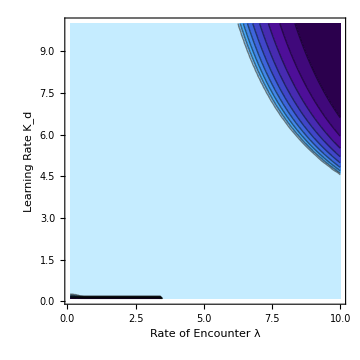

```mathematica
data=Flatten[<<"datakdλ1",1];
kdλ1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .05; Row 1

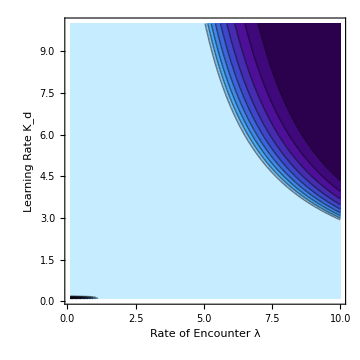

```mathematica
data=Flatten[<<"datakdλ2",1];
kdλ2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .08; Row 1

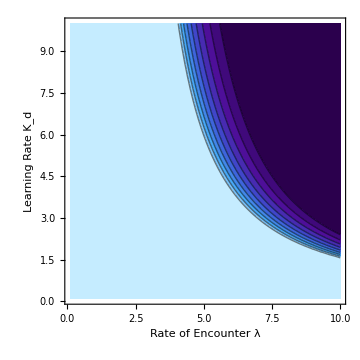

```mathematica
data=Flatten[<<"datakdλcL3",1];
kdλ3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Learning Rate K_d",Black,20]]},ColorFunction->("DeepSeaColors")]
```

### Row 2

#### Δ = .02; Row 2

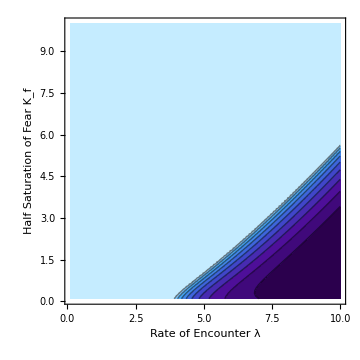

```mathematica
data=Flatten[<<"datakfλ1",1];
kfλ1=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .05; Row 2

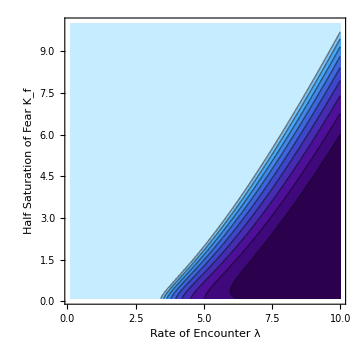

```mathematica
data=Flatten[<<"datakfλ2",1];
kfλ2=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### Δ = .08; Row 2

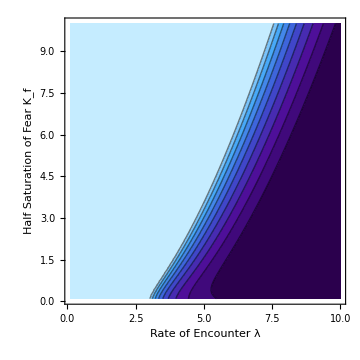

```mathematica
data=Flatten[<<"datakfλ3",1];
kfλ3=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,14],ImageSize->Medium,FrameLabel->{Text[Style["Rate of Encounter λ",Black,20]],Text[Style["Half Saturation of Fear K_f",Black,20]]},ColorFunction->("DeepSeaColors")]
```

### Grid

```mathematica
costgrid=Grid[{{Text[Style["   Δ 0.02",20,TextAlignment->Center]],Text[Style["    Δ 0.05",20,TextAlignment->Center]],Text[Style["     Δ 0.08",20,TextAlignment->Center]]},{kdλ3,kdλ2,kdλ1},{kfλ3,kfλ2,kfλ1}}]
```

Δ 0.02 |     Δ 0.05 |      Δ 0.08
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

## Figure S4

### Data Points

```mathematica
(*data ran on cluster to expedite run time. Functions are copied below the data points for replication purposes*)
```

#### λ = 1

```mathematica
data = {{{0.,0.,1.},{0.01,0.,1.},{0.02,0.,1.},{0.03,0.,1.},{0.04,0.,1.},{0.05,0.,1.},{0.06,0.,1.},{0.07,0.,1.},{0.08,0.,1.},{0.09,0.,1.},{0.1,0.,1.},{0.11,0.,1.},{0.12,0.,1.},{0.13,0.,1.},{0.14,0.,1.},{0.15,0.,1.},{0.16,0.,1.},{0.17,0.,1.},{0.18,0.,1.},{0.19,0.,1.},{0.2,0.,1.},{0.21,0.,1.},{0.22,0.,1.},{0.23,0.,1.},{0.24,0.,1.},{0.25,0.,1.},{0.26,0.,1.},{0.27,0.,1.},{0.28,0.,1.},{0.29,0.,1.},{0.3,0.,1.},{0.31,0.,1.},{0.32,0.,1.},{0.33,0.,1.},{0.34,0.,1.},{0.35000000000000003,0.,1.},{0.36,0.,1.},{0.37,0.,1.},{0.38,0.,1.},{0.39,0.,1.},{0.4,0.,1.},{0.41000000000000003,0.,1.},{0.42,0.,1.},{0.43,0.,1.},{0.44,0.,1.},{0.45,0.,1.},{0.46,0.,1.},{0.47000000000000003,0.,1.},{0.48,0.,1.},{0.49,0.,1.},{0.5,0.,1.},{0.51,0.,1.},{0.52,0.,1.},{0.53,0.,1.},{0.54,0.,1.},{0.55,0.,1.},{0.56,0.,1.},{0.5700000000000001,0.,1.},{0.58,0.,1.},{0.59,0.,1.},{0.6,0.,1.},{0.61,0.,1.},{0.62,0.,1.},{0.63,0.,1.},{0.64,0.,1.},{0.65,0.,1.},{0.66,0.,1.},{0.67,0.,1.},{0.68,0.,1.},{0.6900000000000001,0.,1.},{0.7000000000000001,0.,1.},{0.71,0.,1.},{0.72,0.,1.},{0.73,0.,1.},{0.74,0.,1.},{0.75,0.,1.},{0.76,0.,1.},{0.77,0.,1.},{0.78,0.,1.},{0.79,0.,1.},{0.8,0.,1.},{0.81,0.,1.},{0.8200000000000001,0.,1.},{0.8300000000000001,0.,1.},{0.84,0.,1.},{0.85,0.,1.},{0.86,0.,1.},{0.87,0.,1.},{0.88,0.,1.},{0.89,0.,1.},{0.9,0.,1.},{0.91,0.,1.},{0.92,0.,1.},{0.93,0.,1.},{0.9400000000000001,0.,1.},{0.9500000000000001,0.,1.},{0.96,0.,1.},{0.97,0.,1.},{0.98,0.,1.},{0.99,0.,1.},{1.,0.,1.}},{{0.,0.01,1.},{0.01,0.01,1.},{0.02,0.01,1.},{0.03,0.01,1.},{0.04,0.01,1.},{0.05,0.01,1.},{0.06,0.01,1.},{0.07,0.01,1.},{0.08,0.01,1.},{0.09,0.01,1.},{0.1,0.01,1.},{0.11,0.01,1.},{0.12,0.01,1.},{0.13,0.01,1.},{0.14,0.01,1.},{0.15,0.01,1.},{0.16,0.01,1.},{0.17,0.01,1.},{0.18,0.01,1.},{0.19,0.01,1.},{0.2,0.01,1.},{0.21,0.01,1.},{0.22,0.01,1.},{0.23,0.01,1.},{0.24,0.01,1.},{0.25,0.01,1.},{0.26,0.01,1.},{0.27,0.01,1.},{0.28,0.01,1.},{0.29,0.01,1.},{0.3,0.01,1.},{0.31,0.01,1.},{0.32,0.01,1.},{0.33,0.01,1.},{0.34,0.01,1.},{0.35000000000000003,0.01,1.},{0.36,0.01,1.},{0.37,0.01,1.},{0.38,0.01,1.},{0.39,0.01,1.},{0.4,0.01,1.},{0.41000000000000003,0.01,1.},{0.42,0.01,1.},{0.43,0.01,1.},{0.44,0.01,1.},{0.45,0.01,1.},{0.46,0.01,1.},{0.47000000000000003,0.01,1.},{0.48,0.01,1.},{0.49,0.01,1.},{0.5,0.01,1.},{0.51,0.01,1.},{0.52,0.01,1.},{0.53,0.01,1.},{0.54,0.01,1.},{0.55,0.01,1.},{0.56,0.01,1.},{0.5700000000000001,0.01,1.},{0.58,0.01,1.},{0.59,0.01,1.},{0.6,0.01,1.},{0.61,0.01,1.},{0.62,0.01,1.},{0.63,0.01,1.},{0.64,0.01,1.},{0.65,0.01,1.},{0.66,0.01,1.},{0.67,0.01,1.},{0.68,0.01,1.},{0.6900000000000001,0.01,1.},{0.7000000000000001,0.01,1.},{0.71,0.01,1.},{0.72,0.01,1.},{0.73,0.01,1.},{0.74,0.01,1.},{0.75,0.01,1.},{0.76,0.01,1.},{0.77,0.01,1.},{0.78,0.01,1.},{0.79,0.01,1.},{0.8,0.01,1.},{0.81,0.01,1.},{0.8200000000000001,0.01,1.},{0.8300000000000001,0.01,1.},{0.84,0.01,1.},{0.85,0.01,1.},{0.86,0.01,1.},{0.87,0.01,1.},{0.88,0.01,1.},{0.89,0.01,1.},{0.9,0.01,1.},{0.91,0.01,1.},{0.92,0.01,1.},{0.93,0.01,1.},{0.9400000000000001,0.01,1.},{0.9500000000000001,0.01,1.},{0.96,0.01,1.},{0.97,0.01,1.},{0.98,0.01,1.},{0.99,0.01,1.},{1.,0.01,1.}},{{0.,0.02,1.},{0.01,0.02,1.},{0.02,0.02,1.},{0.03,0.02,1.},{0.04,0.02,1.},{0.05,0.02,1.},{0.06,0.02,1.},{0.07,0.02,1.},{0.08,0.02,1.},{0.09,0.02,1.},{0.1,0.02,1.},{0.11,0.02,1.},{0.12,0.02,1.},{0.13,0.02,1.},{0.14,0.02,1.},{0.15,0.02,1.},{0.16,0.02,1.},{0.17,0.02,1.},{0.18,0.02,1.},{0.19,0.02,1.},{0.2,0.02,1.},{0.21,0.02,1.},{0.22,0.02,1.},{0.23,0.02,1.},{0.24,0.02,1.},{0.25,0.02,1.},{0.26,0.02,1.},{0.27,0.02,1.},{0.28,0.02,1.},{0.29,0.02,1.},{0.3,0.02,1.},{0.31,0.02,1.},{0.32,0.02,1.},{0.33,0.02,1.},{0.34,0.02,1.},{0.35000000000000003,0.02,1.},{0.36,0.02,1.},{0.37,0.02,1.},{0.38,0.02,1.},{0.39,0.02,1.},{0.4,0.02,1.},{0.41000000000000003,0.02,1.},{0.42,0.02,1.},{0.43,0.02,1.},{0.44,0.02,1.},{0.45,0.02,1.},{0.46,0.02,1.},{0.47000000000000003,0.02,1.},{0.48,0.02,1.},{0.49,0.02,1.},{0.5,0.02,1.},{0.51,0.02,1.},{0.52,0.02,1.},{0.53,0.02,1.},{0.54,0.02,1.},{0.55,0.02,1.},{0.56,0.02,1.},{0.5700000000000001,0.02,1.},{0.58,0.02,1.},{0.59,0.02,1.},{0.6,0.02,1.},{0.61,0.02,1.},{0.62,0.02,1.},{0.63,0.02,1.},{0.64,0.02,1.},{0.65,0.02,1.},{0.66,0.02,1.},{0.67,0.02,1.},{0.68,0.02,1.},{0.6900000000000001,0.02,1.},{0.7000000000000001,0.02,1.},{0.71,0.02,1.},{0.72,0.02,1.},{0.73,0.02,1.},{0.74,0.02,1.},{0.75,0.02,1.},{0.76,0.02,1.},{0.77,0.02,1.},{0.78,0.02,1.},{0.79,0.02,1.},{0.8,0.02,1.},{0.81,0.02,1.},{0.8200000000000001,0.02,1.},{0.8300000000000001,0.02,1.},{0.84,0.02,1.},{0.85,0.02,1.},{0.86,0.02,1.},{0.87,0.02,1.},{0.88,0.02,1.},{0.89,0.02,1.},{0.9,0.02,1.},{0.91,0.02,1.},{0.92,0.02,1.},{0.93,0.02,1.},{0.9400000000000001,0.02,1.},{0.9500000000000001,0.02,1.},{0.96,0.02,1.},{0.97,0.02,1.},{0.98,0.02,1.},{0.99,0.02,1.},{1.,0.02,1.}},{{0.,0.03,1.},{0.01,0.03,1.},{0.02,0.03,1.},{0.03,0.03,1.},{0.04,0.03,1.},{0.05,0.03,1.},{0.06,0.03,1.},{0.07,0.03,1.},{0.08,0.03,1.},{0.09,0.03,1.},{0.1,0.03,1.},{0.11,0.03,1.},{0.12,0.03,1.},{0.13,0.03,1.},{0.14,0.03,1.},{0.15,0.03,1.},{0.16,0.03,1.},{0.17,0.03,1.},{0.18,0.03,1.},{0.19,0.03,1.},{0.2,0.03,1.},{0.21,0.03,1.},{0.22,0.03,1.},{0.23,0.03,1.},{0.24,0.03,1.},{0.25,0.03,1.},{0.26,0.03,1.},{0.27,0.03,1.},{0.28,0.03,1.},{0.29,0.03,1.},{0.3,0.03,1.},{0.31,0.03,1.},{0.32,0.03,1.},{0.33,0.03,1.},{0.34,0.03,1.},{0.35000000000000003,0.03,1.},{0.36,0.03,1.},{0.37,0.03,1.},{0.38,0.03,1.},{0.39,0.03,1.},{0.4,0.03,1.},{0.41000000000000003,0.03,1.},{0.42,0.03,1.},{0.43,0.03,1.},{0.44,0.03,1.},{0.45,0.03,1.},{0.46,0.03,1.},{0.47000000000000003,0.03,1.},{0.48,0.03,1.},{0.49,0.03,1.},{0.5,0.03,1.},{0.51,0.03,1.},{0.52,0.03,1.},{0.53,0.03,1.},{0.54,0.03,1.},{0.55,0.03,1.},{0.56,0.03,1.},{0.5700000000000001,0.03,1.},{0.58,0.03,1.},{0.59,0.03,1.},{0.6,0.03,1.},{0.61,0.03,1.},{0.62,0.03,1.},{0.63,0.03,1.},{0.64,0.03,1.},{0.65,0.03,1.},{0.66,0.03,1.},{0.67,0.03,1.},{0.68,0.03,1.},{0.6900000000000001,0.03,1.},{0.7000000000000001,0.03,1.},{0.71,0.03,1.},{0.72,0.03,1.},{0.73,0.03,1.},{0.74,0.03,1.},{0.75,0.03,1.},{0.76,0.03,1.},{0.77,0.03,1.},{0.78,0.03,1.},{0.79,0.03,1.},{0.8,0.03,1.},{0.81,0.03,1.},{0.8200000000000001,0.03,1.},{0.8300000000000001,0.03,1.},{0.84,0.03,1.},{0.85,0.03,1.},{0.86,0.03,1.},{0.87,0.03,1.},{0.88,0.03,1.},{0.89,0.03,1.},{0.9,0.03,1.},{0.91,0.03,1.},{0.92,0.03,1.},{0.93,0.03,1.},{0.9400000000000001,0.03,1.},{0.9500000000000001,0.03,1.},{0.96,0.03,1.},{0.97,0.03,1.},{0.98,0.03,1.},{0.99,0.03,1.},{1.,0.03,1.}},{{0.,0.04,1.},{0.01,0.04,1.},{0.02,0.04,1.},{0.03,0.04,1.},{0.04,0.04,1.},{0.05,0.04,1.},{0.06,0.04,1.},{0.07,0.04,1.},{0.08,0.04,1.},{0.09,0.04,1.},{0.1,0.04,1.},{0.11,0.04,1.},{0.12,0.04,1.},{0.13,0.04,1.},{0.14,0.04,1.},{0.15,0.04,1.},{0.16,0.04,1.},{0.17,0.04,1.},{0.18,0.04,1.},{0.19,0.04,1.},{0.2,0.04,1.},{0.21,0.04,1.},{0.22,0.04,1.},{0.23,0.04,1.},{0.24,0.04,1.},{0.25,0.04,1.},{0.26,0.04,1.},{0.27,0.04,1.},{0.28,0.04,1.},{0.29,0.04,1.},{0.3,0.04,1.},{0.31,0.04,1.},{0.32,0.04,1.},{0.33,0.04,1.},{0.34,0.04,1.},{0.35000000000000003,0.04,1.},{0.36,0.04,1.},{0.37,0.04,1.},{0.38,0.04,1.},{0.39,0.04,1.},{0.4,0.04,1.},{0.41000000000000003,0.04,1.},{0.42,0.04,1.},{0.43,0.04,1.},{0.44,0.04,1.},{0.45,0.04,1.},{0.46,0.04,1.},{0.47000000000000003,0.04,1.},{0.48,0.04,1.},{0.49,0.04,1.},{0.5,0.04,1.},{0.51,0.04,1.},{0.52,0.04,1.},{0.53,0.04,1.},{0.54,0.04,1.},{0.55,0.04,1.},{0.56,0.04,1.},{0.5700000000000001,0.04,1.},{0.58,0.04,1.},{0.59,0.04,1.},{0.6,0.04,1.},{0.61,0.04,1.},{0.62,0.04,1.},{0.63,0.04,1.},{0.64,0.04,1.},{0.65,0.04,1.},{0.66,0.04,1.},{0.67,0.04,1.},{0.68,0.04,1.},{0.6900000000000001,0.04,1.},{0.7000000000000001,0.04,1.},{0.71,0.04,1.},{0.72,0.04,1.},{0.73,0.04,1.},{0.74,0.04,1.},{0.75,0.04,1.},{0.76,0.04,1.},{0.77,0.04,1.},{0.78,0.04,1.},{0.79,0.04,1.},{0.8,0.04,1.},{0.81,0.04,1.},{0.8200000000000001,0.04,1.},{0.8300000000000001,0.04,1.},{0.84,0.04,1.},{0.85,0.04,1.},{0.86,0.04,1.},{0.87,0.04,1.},{0.88,0.04,1.},{0.89,0.04,1.},{0.9,0.04,1.},{0.91,0.04,1.},{0.92,0.04,1.},{0.93,0.04,1.},{0.9400000000000001,0.04,1.},{0.9500000000000001,0.04,1.},{0.96,0.04,1.},{0.97,0.04,1.},{0.98,0.04,1.},{0.99,0.04,1.},{1.,0.04,1.}},{{0.,0.05,1.},{0.01,0.05,1.},{0.02,0.05,1.},{0.03,0.05,1.},{0.04,0.05,1.},{0.05,0.05,1.},{0.06,0.05,1.},{0.07,0.05,1.},{0.08,0.05,1.},{0.09,0.05,1.},{0.1,0.05,1.},{0.11,0.05,1.},{0.12,0.05,1.},{0.13,0.05,1.},{0.14,0.05,1.},{0.15,0.05,1.},{0.16,0.05,1.},{0.17,0.05,1.},{0.18,0.05,1.},{0.19,0.05,1.},{0.2,0.05,1.},{0.21,0.05,1.},{0.22,0.05,1.},{0.23,0.05,1.},{0.24,0.05,1.},{0.25,0.05,1.},{0.26,0.05,1.},{0.27,0.05,1.},{0.28,0.05,1.},{0.29,0.05,1.},{0.3,0.05,1.},{0.31,0.05,1.},{0.32,0.05,1.},{0.33,0.05,1.},{0.34,0.05,1.},{0.35000000000000003,0.05,1.},{0.36,0.05,1.},{0.37,0.05,1.},{0.38,0.05,1.},{0.39,0.05,1.},{0.4,0.05,1.},{0.41000000000000003,0.05,1.},{0.42,0.05,1.},{0.43,0.05,1.},{0.44,0.05,1.},{0.45,0.05,1.},{0.46,0.05,1.},{0.47000000000000003,0.05,1.},{0.48,0.05,1.},{0.49,0.05,1.},{0.5,0.05,1.},{0.51,0.05,1.},{0.52,0.05,1.},{0.53,0.05,1.},{0.54,0.05,1.},{0.55,0.05,1.},{0.56,0.05,1.},{0.5700000000000001,0.05,1.},{0.58,0.05,1.},{0.59,0.05,1.},{0.6,0.05,1.},{0.61,0.05,1.},{0.62,0.05,1.},{0.63,0.05,1.},{0.64,0.05,1.},{0.65,0.05,1.},{0.66,0.05,1.},{0.67,0.05,1.},{0.68,0.05,1.},{0.6900000000000001,0.05,1.},{0.7000000000000001,0.05,1.},{0.71,0.05,1.},{0.72,0.05,1.},{0.73,0.05,1.},{0.74,0.05,1.},{0.75,0.05,1.},{0.76,0.05,1.},{0.77,0.05,1.},{0.78,0.05,1.},{0.79,0.05,1.},{0.8,0.05,1.},{0.81,0.05,1.},{0.8200000000000001,0.05,1.},{0.8300000000000001,0.05,1.},{0.84,0.05,1.},{0.85,0.05,1.},{0.86,0.05,1.},{0.87,0.05,1.},{0.88,0.05,1.},{0.89,0.05,1.},{0.9,0.05,1.},{0.91,0.05,1.},{0.92,0.05,1.},{0.93,0.05,1.},{0.9400000000000001,0.05,1.},{0.9500000000000001,0.05,1.},{0.96,0.05,1.},{0.97,0.05,1.},{0.98,0.05,1.},{0.99,0.05,1.},{1.,0.05,1.}},{{0.,0.06,1.},{0.01,0.06,1.},{0.02,0.06,1.},{0.03,0.06,1.},{0.04,0.06,1.},{0.05,0.06,1.},{0.06,0.06,1.},{0.07,0.06,1.},{0.08,0.06,1.},{0.09,0.06,1.},{0.1,0.06,1.},{0.11,0.06,1.},{0.12,0.06,1.},{0.13,0.06,1.},{0.14,0.06,1.},{0.15,0.06,1.},{0.16,0.06,1.},{0.17,0.06,1.},{0.18,0.06,1.},{0.19,0.06,1.},{0.2,0.06,1.},{0.21,0.06,1.},{0.22,0.06,1.},{0.23,0.06,1.},{0.24,0.06,1.},{0.25,0.06,1.},{0.26,0.06,1.},{0.27,0.06,1.},{0.28,0.06,1.},{0.29,0.06,1.},{0.3,0.06,1.},{0.31,0.06,1.},{0.32,0.06,1.},{0.33,0.06,1.},{0.34,0.06,1.},{0.35000000000000003,0.06,1.},{0.36,0.06,1.},{0.37,0.06,1.},{0.38,0.06,1.},{0.39,0.06,1.},{0.4,0.06,1.},{0.41000000000000003,0.06,1.},{0.42,0.06,1.},{0.43,0.06,1.},{0.44,0.06,1.},{0.45,0.06,1.},{0.46,0.06,1.},{0.47000000000000003,0.06,1.},{0.48,0.06,1.},{0.49,0.06,1.},{0.5,0.06,1.},{0.51,0.06,1.},{0.52,0.06,1.},{0.53,0.06,1.},{0.54,0.06,1.},{0.55,0.06,1.},{0.56,0.06,1.},{0.5700000000000001,0.06,1.},{0.58,0.06,1.},{0.59,0.06,1.},{0.6,0.06,1.},{0.61,0.06,1.},{0.62,0.06,1.},{0.63,0.06,1.},{0.64,0.06,1.},{0.65,0.06,1.},{0.66,0.06,1.},{0.67,0.06,1.},{0.68,0.06,1.},{0.6900000000000001,0.06,1.},{0.7000000000000001,0.06,1.},{0.71,0.06,1.},{0.72,0.06,1.},{0.73,0.06,1.},{0.74,0.06,1.},{0.75,0.06,1.},{0.76,0.06,1.},{0.77,0.06,1.},{0.78,0.06,1.},{0.79,0.06,1.},{0.8,0.06,1.},{0.81,0.06,1.},{0.8200000000000001,0.06,1.},{0.8300000000000001,0.06,1.},{0.84,0.06,1.},{0.85,0.06,1.},{0.86,0.06,1.},{0.87,0.06,1.},{0.88,0.06,1.},{0.89,0.06,1.},{0.9,0.06,1.},{0.91,0.06,1.},{0.92,0.06,1.},{0.93,0.06,1.},{0.9400000000000001,0.06,1.},{0.9500000000000001,0.06,1.},{0.96,0.06,1.},{0.97,0.06,1.},{0.98,0.06,1.},{0.99,0.06,1.},{1.,0.06,1.}},{{0.,0.06999999999999999,1.},{0.01,0.06999999999999999,1.},{0.02,0.06999999999999999,1.},{0.03,0.06999999999999999,1.},{0.04,0.06999999999999999,1.},{0.05,0.06999999999999999,1.},{0.06,0.06999999999999999,1.},{0.07,0.06999999999999999,1.},{0.08,0.06999999999999999,1.},{0.09,0.06999999999999999,1.},{0.1,0.06999999999999999,1.},{0.11,0.06999999999999999,1.},{0.12,0.06999999999999999,1.},{0.13,0.06999999999999999,1.},{0.14,0.06999999999999999,1.},{0.15,0.06999999999999999,1.},{0.16,0.06999999999999999,1.},{0.17,0.06999999999999999,1.},{0.18,0.06999999999999999,1.},{0.19,0.06999999999999999,1.},{0.2,0.06999999999999999,1.},{0.21,0.06999999999999999,1.},{0.22,0.06999999999999999,1.},{0.23,0.06999999999999999,1.},{0.24,0.06999999999999999,1.},{0.25,0.06999999999999999,1.},{0.26,0.06999999999999999,1.},{0.27,0.06999999999999999,1.},{0.28,0.06999999999999999,1.},{0.29,0.06999999999999999,1.},{0.3,0.06999999999999999,1.},{0.31,0.06999999999999999,1.},{0.32,0.06999999999999999,1.},{0.33,0.06999999999999999,1.},{0.34,0.06999999999999999,1.},{0.35000000000000003,0.06999999999999999,1.},{0.36,0.06999999999999999,1.},{0.37,0.06999999999999999,1.},{0.38,0.06999999999999999,1.},{0.39,0.06999999999999999,1.},{0.4,0.06999999999999999,1.},{0.41000000000000003,0.06999999999999999,1.},{0.42,0.06999999999999999,1.},{0.43,0.06999999999999999,1.},{0.44,0.06999999999999999,1.},{0.45,0.06999999999999999,1.},{0.46,0.06999999999999999,1.},{0.47000000000000003,0.06999999999999999,1.},{0.48,0.06999999999999999,1.},{0.49,0.06999999999999999,1.},{0.5,0.06999999999999999,1.},{0.51,0.06999999999999999,1.},{0.52,0.06999999999999999,1.},{0.53,0.06999999999999999,1.},{0.54,0.06999999999999999,1.},{0.55,0.06999999999999999,1.},{0.56,0.06999999999999999,1.},{0.5700000000000001,0.06999999999999999,1.},{0.58,0.06999999999999999,1.},{0.59,0.06999999999999999,1.},{0.6,0.06999999999999999,1.},{0.61,0.06999999999999999,1.},{0.62,0.06999999999999999,1.},{0.63,0.06999999999999999,1.},{0.64,0.06999999999999999,1.},{0.65,0.06999999999999999,1.},{0.66,0.06999999999999999,1.},{0.67,0.06999999999999999,1.},{0.68,0.06999999999999999,1.},{0.6900000000000001,0.06999999999999999,1.},{0.7000000000000001,0.06999999999999999,1.},{0.71,0.06999999999999999,1.},{0.72,0.06999999999999999,1.},{0.73,0.06999999999999999,1.},{0.74,0.06999999999999999,1.},{0.75,0.06999999999999999,1.},{0.76,0.06999999999999999,1.},{0.77,0.06999999999999999,1.},{0.78,0.06999999999999999,1.},{0.79,0.06999999999999999,1.},{0.8,0.06999999999999999,1.},{0.81,0.06999999999999999,1.},{0.8200000000000001,0.06999999999999999,1.},{0.8300000000000001,0.06999999999999999,1.},{0.84,0.06999999999999999,1.},{0.85,0.06999999999999999,1.},{0.86,0.06999999999999999,1.},{0.87,0.06999999999999999,1.},{0.88,0.06999999999999999,1.},{0.89,0.06999999999999999,1.},{0.9,0.06999999999999999,1.},{0.91,0.06999999999999999,1.},{0.92,0.06999999999999999,1.},{0.93,0.06999999999999999,1.},{0.9400000000000001,0.06999999999999999,1.},{0.9500000000000001,0.06999999999999999,1.},{0.96,0.06999999999999999,1.},{0.97,0.06999999999999999,1.},{0.98,0.06999999999999999,1.},{0.99,0.06999999999999999,1.},{1.,0.06999999999999999,1.}},{{0.,0.08,1.},{0.01,0.08,1.},{0.02,0.08,1.},{0.03,0.08,1.},{0.04,0.08,1.},{0.05,0.08,1.},{0.06,0.08,1.},{0.07,0.08,1.},{0.08,0.08,1.},{0.09,0.08,1.},{0.1,0.08,1.},{0.11,0.08,1.},{0.12,0.08,1.},{0.13,0.08,1.},{0.14,0.08,1.},{0.15,0.08,1.},{0.16,0.08,1.},{0.17,0.08,1.},{0.18,0.08,1.},{0.19,0.08,1.},{0.2,0.08,1.},{0.21,0.08,1.},{0.22,0.08,1.},{0.23,0.08,1.},{0.24,0.08,1.},{0.25,0.08,1.},{0.26,0.08,1.},{0.27,0.08,1.},{0.28,0.08,1.},{0.29,0.08,1.},{0.3,0.08,1.},{0.31,0.08,1.},{0.32,0.08,1.},{0.33,0.08,1.},{0.34,0.08,1.},{0.35000000000000003,0.08,1.},{0.36,0.08,1.},{0.37,0.08,1.},{0.38,0.08,1.},{0.39,0.08,1.},{0.4,0.08,1.},{0.41000000000000003,0.08,1.},{0.42,0.08,1.},{0.43,0.08,1.},{0.44,0.08,1.},{0.45,0.08,1.},{0.46,0.08,1.},{0.47000000000000003,0.08,1.},{0.48,0.08,1.},{0.49,0.08,1.},{0.5,0.08,1.},{0.51,0.08,1.},{0.52,0.08,1.},{0.53,0.08,1.},{0.54,0.08,1.},{0.55,0.08,1.},{0.56,0.08,1.},{0.5700000000000001,0.08,1.},{0.58,0.08,1.},{0.59,0.08,1.},{0.6,0.08,1.},{0.61,0.08,1.},{0.62,0.08,1.},{0.63,0.08,1.},{0.64,0.08,1.},{0.65,0.08,1.},{0.66,0.08,1.},{0.67,0.08,1.},{0.68,0.08,1.},{0.6900000000000001,0.08,1.},{0.7000000000000001,0.08,1.},{0.71,0.08,1.},{0.72,0.08,1.},{0.73,0.08,1.},{0.74,0.08,1.},{0.75,0.08,1.},{0.76,0.08,1.},{0.77,0.08,1.},{0.78,0.08,1.},{0.79,0.08,1.},{0.8,0.08,1.},{0.81,0.08,1.},{0.8200000000000001,0.08,1.},{0.8300000000000001,0.08,1.},{0.84,0.08,1.},{0.85,0.08,1.},{0.86,0.08,1.},{0.87,0.08,1.},{0.88,0.08,1.},{0.89,0.08,1.},{0.9,0.08,1.},{0.91,0.08,1.},{0.92,0.08,1.},{0.93,0.08,1.},{0.9400000000000001,0.08,1.},{0.9500000000000001,0.08,1.},{0.96,0.08,1.},{0.97,0.08,1.},{0.98,0.08,1.},{0.99,0.08,1.},{1.,0.08,1.}},{{0.,0.09,1.},{0.01,0.09,1.},{0.02,0.09,1.},{0.03,0.09,1.},{0.04,0.09,1.},{0.05,0.09,1.},{0.06,0.09,1.},{0.07,0.09,1.},{0.08,0.09,1.},{0.09,0.09,1.},{0.1,0.09,1.},{0.11,0.09,1.},{0.12,0.09,1.},{0.13,0.09,1.},{0.14,0.09,1.},{0.15,0.09,1.},{0.16,0.09,1.},{0.17,0.09,1.},{0.18,0.09,1.},{0.19,0.09,1.},{0.2,0.09,1.},{0.21,0.09,1.},{0.22,0.09,1.},{0.23,0.09,1.},{0.24,0.09,1.},{0.25,0.09,1.},{0.26,0.09,1.},{0.27,0.09,1.},{0.28,0.09,1.},{0.29,0.09,1.},{0.3,0.09,1.},{0.31,0.09,1.},{0.32,0.09,1.},{0.33,0.09,1.},{0.34,0.09,1.},{0.35000000000000003,0.09,1.},{0.36,0.09,1.},{0.37,0.09,1.},{0.38,0.09,1.},{0.39,0.09,1.},{0.4,0.09,1.},{0.41000000000000003,0.09,1.},{0.42,0.09,1.},{0.43,0.09,1.},{0.44,0.09,1.},{0.45,0.09,1.},{0.46,0.09,1.},{0.47000000000000003,0.09,1.},{0.48,0.09,1.},{0.49,0.09,1.},{0.5,0.09,1.},{0.51,0.09,1.},{0.52,0.09,1.},{0.53,0.09,1.},{0.54,0.09,1.},{0.55,0.09,1.},{0.56,0.09,1.},{0.5700000000000001,0.09,1.},{0.58,0.09,1.},{0.59,0.09,1.},{0.6,0.09,1.},{0.61,0.09,1.},{0.62,0.09,1.},{0.63,0.09,1.},{0.64,0.09,1.},{0.65,0.09,1.},{0.66,0.09,1.},{0.67,0.09,1.},{0.68,0.09,1.},{0.6900000000000001,0.09,1.},{0.7000000000000001,0.09,1.},{0.71,0.09,1.},{0.72,0.09,1.},{0.73,0.09,1.},{0.74,0.09,1.},{0.75,0.09,1.},{0.76,0.09,1.},{0.77,0.09,1.},{0.78,0.09,1.},{0.79,0.09,1.},{0.8,0.09,1.},{0.81,0.09,1.},{0.8200000000000001,0.09,1.},{0.8300000000000001,0.09,1.},{0.84,0.09,1.},{0.85,0.09,1.},{0.86,0.09,1.},{0.87,0.09,1.},{0.88,0.09,1.},{0.89,0.09,1.},{0.9,0.09,1.},{0.91,0.09,1.},{0.92,0.09,1.},{0.93,0.09,1.},{0.9400000000000001,0.09,1.},{0.9500000000000001,0.09,1.},{0.96,0.09,1.},{0.97,0.09,1.},{0.98,0.09,1.},{0.99,0.09,1.},{1.,0.09,1.}},{{0.,0.09999999999999999,1.},{0.01,0.09999999999999999,1.},{0.02,0.09999999999999999,1.},{0.03,0.09999999999999999,1.},{0.04,0.09999999999999999,1.},{0.05,0.09999999999999999,1.},{0.06,0.09999999999999999,1.},{0.07,0.09999999999999999,1.},{0.08,0.09999999999999999,1.},{0.09,0.09999999999999999,1.},{0.1,0.09999999999999999,1.},{0.11,0.09999999999999999,1.},{0.12,0.09999999999999999,1.},{0.13,0.09999999999999999,1.},{0.14,0.09999999999999999,1.},{0.15,0.09999999999999999,1.},{0.16,0.09999999999999999,1.},{0.17,0.09999999999999999,1.},{0.18,0.09999999999999999,1.},{0.19,0.09999999999999999,1.},{0.2,0.09999999999999999,1.},{0.21,0.09999999999999999,1.},{0.22,0.09999999999999999,1.},{0.23,0.09999999999999999,1.},{0.24,0.09999999999999999,1.},{0.25,0.09999999999999999,1.},{0.26,0.09999999999999999,1.},{0.27,0.09999999999999999,1.},{0.28,0.09999999999999999,1.},{0.29,0.09999999999999999,1.},{0.3,0.09999999999999999,1.},{0.31,0.09999999999999999,1.},{0.32,0.09999999999999999,1.},{0.33,0.09999999999999999,1.},{0.34,0.09999999999999999,1.},{0.35000000000000003,0.09999999999999999,1.},{0.36,0.09999999999999999,1.},{0.37,0.09999999999999999,1.},{0.38,0.09999999999999999,1.},{0.39,0.09999999999999999,1.},{0.4,0.09999999999999999,1.},{0.41000000000000003,0.09999999999999999,1.},{0.42,0.09999999999999999,1.},{0.43,0.09999999999999999,1.},{0.44,0.09999999999999999,1.},{0.45,0.09999999999999999,1.},{0.46,0.09999999999999999,1.},{0.47000000000000003,0.09999999999999999,1.},{0.48,0.09999999999999999,1.},{0.49,0.09999999999999999,1.},{0.5,0.09999999999999999,1.},{0.51,0.09999999999999999,1.},{0.52,0.09999999999999999,1.},{0.53,0.09999999999999999,1.},{0.54,0.09999999999999999,1.},{0.55,0.09999999999999999,1.},{0.56,0.09999999999999999,1.},{0.5700000000000001,0.09999999999999999,1.},{0.58,0.09999999999999999,1.},{0.59,0.09999999999999999,1.},{0.6,0.09999999999999999,1.},{0.61,0.09999999999999999,1.},{0.62,0.09999999999999999,1.},{0.63,0.09999999999999999,1.},{0.64,0.09999999999999999,1.},{0.65,0.09999999999999999,1.},{0.66,0.09999999999999999,1.},{0.67,0.09999999999999999,1.},{0.68,0.09999999999999999,1.},{0.6900000000000001,0.09999999999999999,1.},{0.7000000000000001,0.09999999999999999,1.},{0.71,0.09999999999999999,1.},{0.72,0.09999999999999999,1.},{0.73,0.09999999999999999,1.},{0.74,0.09999999999999999,1.},{0.75,0.09999999999999999,1.},{0.76,0.09999999999999999,1.},{0.77,0.09999999999999999,1.},{0.78,0.09999999999999999,1.},{0.79,0.09999999999999999,1.},{0.8,0.09999999999999999,1.},{0.81,0.09999999999999999,1.},{0.8200000000000001,0.09999999999999999,1.},{0.8300000000000001,0.09999999999999999,1.},{0.84,0.09999999999999999,1.},{0.85,0.09999999999999999,1.},{0.86,0.09999999999999999,1.},{0.87,0.09999999999999999,1.},{0.88,0.09999999999999999,1.},{0.89,0.09999999999999999,1.},{0.9,0.09999999999999999,1.},{0.91,0.09999999999999999,1.},{0.92,0.09999999999999999,1.},{0.93,0.09999999999999999,1.},{0.9400000000000001,0.09999999999999999,1.},{0.9500000000000001,0.09999999999999999,1.},{0.96,0.09999999999999999,1.},{0.97,0.09999999999999999,1.},{0.98,0.09999999999999999,1.},{0.99,0.09999999999999999,1.},{1.,0.09999999999999999,1.}},{{0.,0.11,1.},{0.01,0.11,1.},{0.02,0.11,1.},{0.03,0.11,1.},{0.04,0.11,1.},{0.05,0.11,1.},{0.06,0.11,1.},{0.07,0.11,1.},{0.08,0.11,1.},{0.09,0.11,1.},{0.1,0.11,1.},{0.11,0.11,1.},{0.12,0.11,1.},{0.13,0.11,1.},{0.14,0.11,1.},{0.15,0.11,1.},{0.16,0.11,1.},{0.17,0.11,1.},{0.18,0.11,1.},{0.19,0.11,1.},{0.2,0.11,1.},{0.21,0.11,1.},{0.22,0.11,1.},{0.23,0.11,1.},{0.24,0.11,1.},{0.25,0.11,1.},{0.26,0.11,1.},{0.27,0.11,1.},{0.28,0.11,1.},{0.29,0.11,1.},{0.3,0.11,1.},{0.31,0.11,1.},{0.32,0.11,1.},{0.33,0.11,1.},{0.34,0.11,1.},{0.35000000000000003,0.11,1.},{0.36,0.11,1.},{0.37,0.11,1.},{0.38,0.11,1.},{0.39,0.11,1.},{0.4,0.11,1.},{0.41000000000000003,0.11,1.},{0.42,0.11,1.},{0.43,0.11,1.},{0.44,0.11,1.},{0.45,0.11,1.},{0.46,0.11,1.},{0.47000000000000003,0.11,1.},{0.48,0.11,1.},{0.49,0.11,1.},{0.5,0.11,1.},{0.51,0.11,1.},{0.52,0.11,1.},{0.53,0.11,1.},{0.54,0.11,1.},{0.55,0.11,1.},{0.56,0.11,1.},{0.5700000000000001,0.11,1.},{0.58,0.11,1.},{0.59,0.11,1.},{0.6,0.11,1.},{0.61,0.11,1.},{0.62,0.11,1.},{0.63,0.11,1.},{0.64,0.11,1.},{0.65,0.11,1.},{0.66,0.11,1.},{0.67,0.11,1.},{0.68,0.11,1.},{0.6900000000000001,0.11,1.},{0.7000000000000001,0.11,1.},{0.71,0.11,1.},{0.72,0.11,1.},{0.73,0.11,1.},{0.74,0.11,1.},{0.75,0.11,1.},{0.76,0.11,1.},{0.77,0.11,1.},{0.78,0.11,1.},{0.79,0.11,1.},{0.8,0.11,1.},{0.81,0.11,1.},{0.8200000000000001,0.11,1.},{0.8300000000000001,0.11,1.},{0.84,0.11,1.},{0.85,0.11,1.},{0.86,0.11,1.},{0.87,0.11,1.},{0.88,0.11,1.},{0.89,0.11,1.},{0.9,0.11,1.},{0.91,0.11,1.},{0.92,0.11,1.},{0.93,0.11,1.},{0.9400000000000001,0.11,1.},{0.9500000000000001,0.11,1.},{0.96,0.11,1.},{0.97,0.11,1.},{0.98,0.11,1.},{0.99,0.11,1.},{1.,0.11,1.}},{{0.,0.12,1.},{0.01,0.12,1.},{0.02,0.12,1.},{0.03,0.12,1.},{0.04,0.12,1.},{0.05,0.12,1.},{0.06,0.12,1.},{0.07,0.12,1.},{0.08,0.12,1.},{0.09,0.12,1.},{0.1,0.12,1.},{0.11,0.12,1.},{0.12,0.12,1.},{0.13,0.12,1.},{0.14,0.12,1.},{0.15,0.12,1.},{0.16,0.12,1.},{0.17,0.12,1.},{0.18,0.12,1.},{0.19,0.12,1.},{0.2,0.12,1.},{0.21,0.12,1.},{0.22,0.12,1.},{0.23,0.12,1.},{0.24,0.12,1.},{0.25,0.12,1.},{0.26,0.12,1.},{0.27,0.12,1.},{0.28,0.12,1.},{0.29,0.12,1.},{0.3,0.12,1.},{0.31,0.12,1.},{0.32,0.12,1.},{0.33,0.12,1.},{0.34,0.12,1.},{0.35000000000000003,0.12,1.},{0.36,0.12,1.},{0.37,0.12,1.},{0.38,0.12,1.},{0.39,0.12,1.},{0.4,0.12,1.},{0.41000000000000003,0.12,1.},{0.42,0.12,1.},{0.43,0.12,1.},{0.44,0.12,1.},{0.45,0.12,1.},{0.46,0.12,1.},{0.47000000000000003,0.12,1.},{0.48,0.12,1.},{0.49,0.12,1.},{0.5,0.12,1.},{0.51,0.12,1.},{0.52,0.12,1.},{0.53,0.12,1.},{0.54,0.12,1.},{0.55,0.12,1.},{0.56,0.12,1.},{0.5700000000000001,0.12,1.},{0.58,0.12,1.},{0.59,0.12,1.},{0.6,0.12,1.},{0.61,0.12,1.},{0.62,0.12,1.},{0.63,0.12,1.},{0.64,0.12,1.},{0.65,0.12,1.},{0.66,0.12,1.},{0.67,0.12,1.},{0.68,0.12,1.},{0.6900000000000001,0.12,1.},{0.7000000000000001,0.12,1.},{0.71,0.12,1.},{0.72,0.12,1.},{0.73,0.12,1.},{0.74,0.12,1.},{0.75,0.12,1.},{0.76,0.12,1.},{0.77,0.12,1.},{0.78,0.12,1.},{0.79,0.12,1.},{0.8,0.12,1.},{0.81,0.12,1.},{0.8200000000000001,0.12,1.},{0.8300000000000001,0.12,1.},{0.84,0.12,1.},{0.85,0.12,1.},{0.86,0.12,1.},{0.87,0.12,1.},{0.88,0.12,1.},{0.89,0.12,1.},{0.9,0.12,1.},{0.91,0.12,1.},{0.92,0.12,1.},{0.93,0.12,1.},{0.9400000000000001,0.12,1.},{0.9500000000000001,0.12,1.},{0.96,0.12,1.},{0.97,0.12,1.},{0.98,0.12,1.},{0.99,0.12,1.},{1.,0.12,1.}},{{0.,0.13,1.},{0.01,0.13,1.},{0.02,0.13,1.},{0.03,0.13,1.},{0.04,0.13,1.},{0.05,0.13,1.},{0.06,0.13,1.},{0.07,0.13,1.},{0.08,0.13,1.},{0.09,0.13,1.},{0.1,0.13,1.},{0.11,0.13,1.},{0.12,0.13,1.},{0.13,0.13,1.},{0.14,0.13,1.},{0.15,0.13,1.},{0.16,0.13,1.},{0.17,0.13,1.},{0.18,0.13,1.},{0.19,0.13,1.},{0.2,0.13,1.},{0.21,0.13,1.},{0.22,0.13,1.},{0.23,0.13,1.},{0.24,0.13,1.},{0.25,0.13,1.},{0.26,0.13,1.},{0.27,0.13,1.},{0.28,0.13,1.},{0.29,0.13,1.},{0.3,0.13,1.},{0.31,0.13,1.},{0.32,0.13,1.},{0.33,0.13,1.},{0.34,0.13,1.},{0.35000000000000003,0.13,1.},{0.36,0.13,1.},{0.37,0.13,1.},{0.38,0.13,1.},{0.39,0.13,1.},{0.4,0.13,1.},{0.41000000000000003,0.13,1.},{0.42,0.13,1.},{0.43,0.13,1.},{0.44,0.13,1.},{0.45,0.13,1.},{0.46,0.13,1.},{0.47000000000000003,0.13,1.},{0.48,0.13,1.},{0.49,0.13,1.},{0.5,0.13,1.},{0.51,0.13,1.},{0.52,0.13,1.},{0.53,0.13,1.},{0.54,0.13,1.},{0.55,0.13,1.},{0.56,0.13,1.},{0.5700000000000001,0.13,1.},{0.58,0.13,1.},{0.59,0.13,1.},{0.6,0.13,1.},{0.61,0.13,1.},{0.62,0.13,1.},{0.63,0.13,1.},{0.64,0.13,1.},{0.65,0.13,1.},{0.66,0.13,1.},{0.67,0.13,1.},{0.68,0.13,1.},{0.6900000000000001,0.13,1.},{0.7000000000000001,0.13,1.},{0.71,0.13,1.},{0.72,0.13,1.},{0.73,0.13,1.},{0.74,0.13,1.},{0.75,0.13,1.},{0.76,0.13,1.},{0.77,0.13,1.},{0.78,0.13,1.},{0.79,0.13,1.},{0.8,0.13,1.},{0.81,0.13,1.},{0.8200000000000001,0.13,1.},{0.8300000000000001,0.13,1.},{0.84,0.13,1.},{0.85,0.13,1.},{0.86,0.13,1.},{0.87,0.13,1.},{0.88,0.13,1.},{0.89,0.13,1.},{0.9,0.13,1.},{0.91,0.13,1.},{0.92,0.13,1.},{0.93,0.13,1.},{0.9400000000000001,0.13,1.},{0.9500000000000001,0.13,1.},{0.96,0.13,1.},{0.97,0.13,1.},{0.98,0.13,1.},{0.99,0.13,1.},{1.,0.13,1.}},{{0.,0.13999999999999999,1.},{0.01,0.13999999999999999,1.},{0.02,0.13999999999999999,1.},{0.03,0.13999999999999999,1.},{0.04,0.13999999999999999,1.},{0.05,0.13999999999999999,1.},{0.06,0.13999999999999999,1.},{0.07,0.13999999999999999,1.},{0.08,0.13999999999999999,1.},{0.09,0.13999999999999999,1.},{0.1,0.13999999999999999,1.},{0.11,0.13999999999999999,1.},{0.12,0.13999999999999999,1.},{0.13,0.13999999999999999,1.},{0.14,0.13999999999999999,1.},{0.15,0.13999999999999999,1.},{0.16,0.13999999999999999,1.},{0.17,0.13999999999999999,1.},{0.18,0.13999999999999999,1.},{0.19,0.13999999999999999,1.},{0.2,0.13999999999999999,1.},{0.21,0.13999999999999999,1.},{0.22,0.13999999999999999,1.},{0.23,0.13999999999999999,1.},{0.24,0.13999999999999999,1.},{0.25,0.13999999999999999,1.},{0.26,0.13999999999999999,1.},{0.27,0.13999999999999999,1.},{0.28,0.13999999999999999,1.},{0.29,0.13999999999999999,1.},{0.3,0.13999999999999999,1.},{0.31,0.13999999999999999,1.},{0.32,0.13999999999999999,1.},{0.33,0.13999999999999999,1.},{0.34,0.13999999999999999,1.},{0.35000000000000003,0.13999999999999999,1.},{0.36,0.13999999999999999,1.},{0.37,0.13999999999999999,1.},{0.38,0.13999999999999999,1.},{0.39,0.13999999999999999,1.},{0.4,0.13999999999999999,1.},{0.41000000000000003,0.13999999999999999,1.},{0.42,0.13999999999999999,1.},{0.43,0.13999999999999999,1.},{0.44,0.13999999999999999,1.},{0.45,0.13999999999999999,1.},{0.46,0.13999999999999999,1.},{0.47000000000000003,0.13999999999999999,1.},{0.48,0.13999999999999999,1.},{0.49,0.13999999999999999,1.},{0.5,0.13999999999999999,1.},{0.51,0.13999999999999999,1.},{0.52,0.13999999999999999,1.},{0.53,0.13999999999999999,1.},{0.54,0.13999999999999999,1.},{0.55,0.13999999999999999,1.},{0.56,0.13999999999999999,1.},{0.5700000000000001,0.13999999999999999,1.},{0.58,0.13999999999999999,1.},{0.59,0.13999999999999999,1.},{0.6,0.13999999999999999,1.},{0.61,0.13999999999999999,1.},{0.62,0.13999999999999999,1.},{0.63,0.13999999999999999,1.},{0.64,0.13999999999999999,1.},{0.65,0.13999999999999999,1.},{0.66,0.13999999999999999,1.},{0.67,0.13999999999999999,1.},{0.68,0.13999999999999999,1.},{0.6900000000000001,0.13999999999999999,1.},{0.7000000000000001,0.13999999999999999,1.},{0.71,0.13999999999999999,1.},{0.72,0.13999999999999999,1.},{0.73,0.13999999999999999,1.},{0.74,0.13999999999999999,1.},{0.75,0.13999999999999999,1.},{0.76,0.13999999999999999,1.},{0.77,0.13999999999999999,1.},{0.78,0.13999999999999999,1.},{0.79,0.13999999999999999,1.},{0.8,0.13999999999999999,1.},{0.81,0.13999999999999999,1.},{0.8200000000000001,0.13999999999999999,1.},{0.8300000000000001,0.13999999999999999,1.},{0.84,0.13999999999999999,1.},{0.85,0.13999999999999999,1.},{0.86,0.13999999999999999,1.},{0.87,0.13999999999999999,1.},{0.88,0.13999999999999999,1.},{0.89,0.13999999999999999,1.},{0.9,0.13999999999999999,1.},{0.91,0.13999999999999999,1.},{0.92,0.13999999999999999,1.},{0.93,0.13999999999999999,1.},{0.9400000000000001,0.13999999999999999,1.},{0.9500000000000001,0.13999999999999999,1.},{0.96,0.13999999999999999,1.},{0.97,0.13999999999999999,1.},{0.98,0.13999999999999999,1.},{0.99,0.13999999999999999,1.},{1.,0.13999999999999999,1.}},{{0.,0.15,1.},{0.01,0.15,1.},{0.02,0.15,1.},{0.03,0.15,1.},{0.04,0.15,1.},{0.05,0.15,1.},{0.06,0.15,1.},{0.07,0.15,1.},{0.08,0.15,1.},{0.09,0.15,1.},{0.1,0.15,1.},{0.11,0.15,1.},{0.12,0.15,1.},{0.13,0.15,1.},{0.14,0.15,1.},{0.15,0.15,1.},{0.16,0.15,1.},{0.17,0.15,1.},{0.18,0.15,1.},{0.19,0.15,1.},{0.2,0.15,1.},{0.21,0.15,1.},{0.22,0.15,1.},{0.23,0.15,1.},{0.24,0.15,1.},{0.25,0.15,1.},{0.26,0.15,1.},{0.27,0.15,1.},{0.28,0.15,1.},{0.29,0.15,1.},{0.3,0.15,1.},{0.31,0.15,1.},{0.32,0.15,1.},{0.33,0.15,1.},{0.34,0.15,1.},{0.35000000000000003,0.15,1.},{0.36,0.15,1.},{0.37,0.15,1.},{0.38,0.15,1.},{0.39,0.15,1.},{0.4,0.15,1.},{0.41000000000000003,0.15,1.},{0.42,0.15,1.},{0.43,0.15,1.},{0.44,0.15,1.},{0.45,0.15,1.},{0.46,0.15,1.},{0.47000000000000003,0.15,1.},{0.48,0.15,1.},{0.49,0.15,1.},{0.5,0.15,1.},{0.51,0.15,1.},{0.52,0.15,1.},{0.53,0.15,1.},{0.54,0.15,1.},{0.55,0.15,1.},{0.56,0.15,1.},{0.5700000000000001,0.15,1.},{0.58,0.15,1.},{0.59,0.15,1.},{0.6,0.15,1.},{0.61,0.15,1.},{0.62,0.15,1.},{0.63,0.15,1.},{0.64,0.15,1.},{0.65,0.15,1.},{0.66,0.15,1.},{0.67,0.15,1.},{0.68,0.15,1.},{0.6900000000000001,0.15,1.},{0.7000000000000001,0.15,1.},{0.71,0.15,1.},{0.72,0.15,1.},{0.73,0.15,1.},{0.74,0.15,1.},{0.75,0.15,1.},{0.76,0.15,1.},{0.77,0.15,1.},{0.78,0.15,1.},{0.79,0.15,1.},{0.8,0.15,1.},{0.81,0.15,1.},{0.8200000000000001,0.15,1.},{0.8300000000000001,0.15,1.},{0.84,0.15,1.},{0.85,0.15,1.},{0.86,0.15,1.},{0.87,0.15,1.},{0.88,0.15,1.},{0.89,0.15,1.},{0.9,0.15,1.},{0.91,0.15,1.},{0.92,0.15,1.},{0.93,0.15,1.},{0.9400000000000001,0.15,1.},{0.9500000000000001,0.15,1.},{0.96,0.15,1.},{0.97,0.15,1.},{0.98,0.15,1.},{0.99,0.15,1.},{1.,0.15,1.}},{{0.,0.16,1.},{0.01,0.16,1.},{0.02,0.16,1.},{0.03,0.16,1.},{0.04,0.16,1.},{0.05,0.16,1.},{0.06,0.16,1.},{0.07,0.16,1.},{0.08,0.16,1.},{0.09,0.16,1.},{0.1,0.16,1.},{0.11,0.16,1.},{0.12,0.16,1.},{0.13,0.16,1.},{0.14,0.16,1.},{0.15,0.16,1.},{0.16,0.16,1.},{0.17,0.16,1.},{0.18,0.16,1.},{0.19,0.16,1.},{0.2,0.16,1.},{0.21,0.16,1.},{0.22,0.16,1.},{0.23,0.16,1.},{0.24,0.16,1.},{0.25,0.16,1.},{0.26,0.16,1.},{0.27,0.16,1.},{0.28,0.16,1.},{0.29,0.16,1.},{0.3,0.16,1.},{0.31,0.16,1.},{0.32,0.16,1.},{0.33,0.16,1.},{0.34,0.16,1.},{0.35000000000000003,0.16,1.},{0.36,0.16,1.},{0.37,0.16,1.},{0.38,0.16,1.},{0.39,0.16,1.},{0.4,0.16,1.},{0.41000000000000003,0.16,1.},{0.42,0.16,1.},{0.43,0.16,1.},{0.44,0.16,1.},{0.45,0.16,1.},{0.46,0.16,1.},{0.47000000000000003,0.16,1.},{0.48,0.16,1.},{0.49,0.16,1.},{0.5,0.16,1.},{0.51,0.16,1.},{0.52,0.16,1.},{0.53,0.16,1.},{0.54,0.16,1.},{0.55,0.16,1.},{0.56,0.16,1.},{0.5700000000000001,0.16,1.},{0.58,0.16,1.},{0.59,0.16,1.},{0.6,0.16,1.},{0.61,0.16,1.},{0.62,0.16,1.},{0.63,0.16,1.},{0.64,0.16,1.},{0.65,0.16,1.},{0.66,0.16,1.},{0.67,0.16,1.},{0.68,0.16,1.},{0.6900000000000001,0.16,1.},{0.7000000000000001,0.16,1.},{0.71,0.16,1.},{0.72,0.16,1.},{0.73,0.16,1.},{0.74,0.16,1.},{0.75,0.16,1.},{0.76,0.16,1.},{0.77,0.16,1.},{0.78,0.16,1.},{0.79,0.16,1.},{0.8,0.16,1.},{0.81,0.16,1.},{0.8200000000000001,0.16,1.},{0.8300000000000001,0.16,1.},{0.84,0.16,1.},{0.85,0.16,1.},{0.86,0.16,1.},{0.87,0.16,1.},{0.88,0.16,1.},{0.89,0.16,1.},{0.9,0.16,1.},{0.91,0.16,1.},{0.92,0.16,1.},{0.93,0.16,1.},{0.9400000000000001,0.16,1.},{0.9500000000000001,0.16,1.},{0.96,0.16,1.},{0.97,0.16,1.},{0.98,0.16,1.},{0.99,0.16,1.},{1.,0.16,1.}},{{0.,0.16999999999999998,1.},{0.01,0.16999999999999998,1.},{0.02,0.16999999999999998,1.},{0.03,0.16999999999999998,1.},{0.04,0.16999999999999998,1.},{0.05,0.16999999999999998,1.},{0.06,0.16999999999999998,1.},{0.07,0.16999999999999998,1.},{0.08,0.16999999999999998,1.},{0.09,0.16999999999999998,1.},{0.1,0.16999999999999998,1.},{0.11,0.16999999999999998,1.},{0.12,0.16999999999999998,1.},{0.13,0.16999999999999998,1.},{0.14,0.16999999999999998,1.},{0.15,0.16999999999999998,1.},{0.16,0.16999999999999998,1.},{0.17,0.16999999999999998,1.},{0.18,0.16999999999999998,1.},{0.19,0.16999999999999998,1.},{0.2,0.16999999999999998,1.},{0.21,0.16999999999999998,1.},{0.22,0.16999999999999998,1.},{0.23,0.16999999999999998,1.},{0.24,0.16999999999999998,1.},{0.25,0.16999999999999998,1.},{0.26,0.16999999999999998,1.},{0.27,0.16999999999999998,1.},{0.28,0.16999999999999998,1.},{0.29,0.16999999999999998,1.},{0.3,0.16999999999999998,1.},{0.31,0.16999999999999998,1.},{0.32,0.16999999999999998,1.},{0.33,0.16999999999999998,1.},{0.34,0.16999999999999998,1.},{0.35000000000000003,0.16999999999999998,1.},{0.36,0.16999999999999998,1.},{0.37,0.16999999999999998,1.},{0.38,0.16999999999999998,1.},{0.39,0.16999999999999998,1.},{0.4,0.16999999999999998,1.},{0.41000000000000003,0.16999999999999998,1.},{0.42,0.16999999999999998,1.},{0.43,0.16999999999999998,1.},{0.44,0.16999999999999998,1.},{0.45,0.16999999999999998,1.},{0.46,0.16999999999999998,1.},{0.47000000000000003,0.16999999999999998,1.},{0.48,0.16999999999999998,1.},{0.49,0.16999999999999998,1.},{0.5,0.16999999999999998,1.},{0.51,0.16999999999999998,1.},{0.52,0.16999999999999998,1.},{0.53,0.16999999999999998,1.},{0.54,0.16999999999999998,1.},{0.55,0.16999999999999998,1.},{0.56,0.16999999999999998,1.},{0.5700000000000001,0.16999999999999998,1.},{0.58,0.16999999999999998,1.},{0.59,0.16999999999999998,1.},{0.6,0.16999999999999998,1.},{0.61,0.16999999999999998,1.},{0.62,0.16999999999999998,1.},{0.63,0.16999999999999998,1.},{0.64,0.16999999999999998,1.},{0.65,0.16999999999999998,1.},{0.66,0.16999999999999998,1.},{0.67,0.16999999999999998,1.},{0.68,0.16999999999999998,1.},{0.6900000000000001,0.16999999999999998,1.},{0.7000000000000001,0.16999999999999998,1.},{0.71,0.16999999999999998,1.},{0.72,0.16999999999999998,1.},{0.73,0.16999999999999998,1.},{0.74,0.16999999999999998,1.},{0.75,0.16999999999999998,1.},{0.76,0.16999999999999998,1.},{0.77,0.16999999999999998,1.},{0.78,0.16999999999999998,1.},{0.79,0.16999999999999998,1.},{0.8,0.16999999999999998,1.},{0.81,0.16999999999999998,1.},{0.8200000000000001,0.16999999999999998,1.},{0.8300000000000001,0.16999999999999998,1.},{0.84,0.16999999999999998,1.},{0.85,0.16999999999999998,1.},{0.86,0.16999999999999998,1.},{0.87,0.16999999999999998,1.},{0.88,0.16999999999999998,1.},{0.89,0.16999999999999998,1.},{0.9,0.16999999999999998,1.},{0.91,0.16999999999999998,1.},{0.92,0.16999999999999998,1.},{0.93,0.16999999999999998,1.},{0.9400000000000001,0.16999999999999998,1.},{0.9500000000000001,0.16999999999999998,1.},{0.96,0.16999999999999998,1.},{0.97,0.16999999999999998,1.},{0.98,0.16999999999999998,1.},{0.99,0.16999999999999998,1.},{1.,0.16999999999999998,1.}},{{0.,0.18,1.},{0.01,0.18,1.},{0.02,0.18,1.},{0.03,0.18,1.},{0.04,0.18,1.},{0.05,0.18,1.},{0.06,0.18,1.},{0.07,0.18,1.},{0.08,0.18,1.},{0.09,0.18,1.},{0.1,0.18,1.},{0.11,0.18,1.},{0.12,0.18,1.},{0.13,0.18,1.},{0.14,0.18,1.},{0.15,0.18,1.},{0.16,0.18,1.},{0.17,0.18,1.},{0.18,0.18,1.},{0.19,0.18,1.},{0.2,0.18,1.},{0.21,0.18,1.},{0.22,0.18,1.},{0.23,0.18,1.},{0.24,0.18,1.},{0.25,0.18,1.},{0.26,0.18,1.},{0.27,0.18,1.},{0.28,0.18,1.},{0.29,0.18,1.},{0.3,0.18,1.},{0.31,0.18,1.},{0.32,0.18,1.},{0.33,0.18,1.},{0.34,0.18,1.},{0.35000000000000003,0.18,1.},{0.36,0.18,1.},{0.37,0.18,1.},{0.38,0.18,1.},{0.39,0.18,1.},{0.4,0.18,1.},{0.41000000000000003,0.18,1.},{0.42,0.18,1.},{0.43,0.18,1.},{0.44,0.18,1.},{0.45,0.18,1.},{0.46,0.18,1.},{0.47000000000000003,0.18,1.},{0.48,0.18,1.},{0.49,0.18,1.},{0.5,0.18,1.},{0.51,0.18,1.},{0.52,0.18,1.},{0.53,0.18,1.},{0.54,0.18,1.},{0.55,0.18,1.},{0.56,0.18,1.},{0.5700000000000001,0.18,1.},{0.58,0.18,1.},{0.59,0.18,1.},{0.6,0.18,1.},{0.61,0.18,1.},{0.62,0.18,1.},{0.63,0.18,1.},{0.64,0.18,1.},{0.65,0.18,1.},{0.66,0.18,1.},{0.67,0.18,1.},{0.68,0.18,1.},{0.6900000000000001,0.18,1.},{0.7000000000000001,0.18,1.},{0.71,0.18,1.},{0.72,0.18,1.},{0.73,0.18,1.},{0.74,0.18,1.},{0.75,0.18,1.},{0.76,0.18,1.},{0.77,0.18,1.},{0.78,0.18,1.},{0.79,0.18,1.},{0.8,0.18,1.},{0.81,0.18,1.},{0.8200000000000001,0.18,1.},{0.8300000000000001,0.18,1.},{0.84,0.18,1.},{0.85,0.18,1.},{0.86,0.18,1.},{0.87,0.18,1.},{0.88,0.18,1.},{0.89,0.18,1.},{0.9,0.18,1.},{0.91,0.18,1.},{0.92,0.18,1.},{0.93,0.18,1.},{0.9400000000000001,0.18,1.},{0.9500000000000001,0.18,1.},{0.96,0.18,1.},{0.97,0.18,1.},{0.98,0.18,1.},{0.99,0.18,1.},{1.,0.18,1.}},{{0.,0.19,1.},{0.01,0.19,1.},{0.02,0.19,1.},{0.03,0.19,1.},{0.04,0.19,1.},{0.05,0.19,1.},{0.06,0.19,1.},{0.07,0.19,1.},{0.08,0.19,1.},{0.09,0.19,1.},{0.1,0.19,1.},{0.11,0.19,1.},{0.12,0.19,1.},{0.13,0.19,1.},{0.14,0.19,1.},{0.15,0.19,1.},{0.16,0.19,1.},{0.17,0.19,1.},{0.18,0.19,1.},{0.19,0.19,1.},{0.2,0.19,1.},{0.21,0.19,1.},{0.22,0.19,1.},{0.23,0.19,1.},{0.24,0.19,1.},{0.25,0.19,1.},{0.26,0.19,1.},{0.27,0.19,1.},{0.28,0.19,1.},{0.29,0.19,1.},{0.3,0.19,1.},{0.31,0.19,1.},{0.32,0.19,1.},{0.33,0.19,1.},{0.34,0.19,1.},{0.35000000000000003,0.19,1.},{0.36,0.19,1.},{0.37,0.19,1.},{0.38,0.19,1.},{0.39,0.19,1.},{0.4,0.19,1.},{0.41000000000000003,0.19,1.},{0.42,0.19,1.},{0.43,0.19,1.},{0.44,0.19,1.},{0.45,0.19,1.},{0.46,0.19,1.},{0.47000000000000003,0.19,1.},{0.48,0.19,1.},{0.49,0.19,1.},{0.5,0.19,1.},{0.51,0.19,1.},{0.52,0.19,1.},{0.53,0.19,1.},{0.54,0.19,1.},{0.55,0.19,1.},{0.56,0.19,1.},{0.5700000000000001,0.19,1.},{0.58,0.19,1.},{0.59,0.19,1.},{0.6,0.19,1.},{0.61,0.19,1.},{0.62,0.19,1.},{0.63,0.19,1.},{0.64,0.19,1.},{0.65,0.19,1.},{0.66,0.19,1.},{0.67,0.19,1.},{0.68,0.19,1.},{0.6900000000000001,0.19,1.},{0.7000000000000001,0.19,1.},{0.71,0.19,1.},{0.72,0.19,1.},{0.73,0.19,1.},{0.74,0.19,1.},{0.75,0.19,1.},{0.76,0.19,1.},{0.77,0.19,1.},{0.78,0.19,1.},{0.79,0.19,1.},{0.8,0.19,1.},{0.81,0.19,1.},{0.8200000000000001,0.19,1.},{0.8300000000000001,0.19,1.},{0.84,0.19,1.},{0.85,0.19,1.},{0.86,0.19,1.},{0.87,0.19,1.},{0.88,0.19,1.},{0.89,0.19,1.},{0.9,0.19,1.},{0.91,0.19,1.},{0.92,0.19,1.},{0.93,0.19,1.},{0.9400000000000001,0.19,1.},{0.9500000000000001,0.19,1.},{0.96,0.19,1.},{0.97,0.19,1.},{0.98,0.19,1.},{0.99,0.19,1.},{1.,0.19,1.}},{{0.,0.19999999999999998,1.},{0.01,0.19999999999999998,1.},{0.02,0.19999999999999998,1.},{0.03,0.19999999999999998,1.},{0.04,0.19999999999999998,1.},{0.05,0.19999999999999998,1.},{0.06,0.19999999999999998,1.},{0.07,0.19999999999999998,1.},{0.08,0.19999999999999998,1.},{0.09,0.19999999999999998,1.},{0.1,0.19999999999999998,1.},{0.11,0.19999999999999998,1.},{0.12,0.19999999999999998,1.},{0.13,0.19999999999999998,1.},{0.14,0.19999999999999998,1.},{0.15,0.19999999999999998,1.},{0.16,0.19999999999999998,1.},{0.17,0.19999999999999998,1.},{0.18,0.19999999999999998,1.},{0.19,0.19999999999999998,1.},{0.2,0.19999999999999998,1.},{0.21,0.19999999999999998,1.},{0.22,0.19999999999999998,1.},{0.23,0.19999999999999998,1.},{0.24,0.19999999999999998,1.},{0.25,0.19999999999999998,1.},{0.26,0.19999999999999998,1.},{0.27,0.19999999999999998,1.},{0.28,0.19999999999999998,1.},{0.29,0.19999999999999998,1.},{0.3,0.19999999999999998,1.},{0.31,0.19999999999999998,1.},{0.32,0.19999999999999998,1.},{0.33,0.19999999999999998,1.},{0.34,0.19999999999999998,1.},{0.35000000000000003,0.19999999999999998,1.},{0.36,0.19999999999999998,1.},{0.37,0.19999999999999998,1.},{0.38,0.19999999999999998,1.},{0.39,0.19999999999999998,1.},{0.4,0.19999999999999998,1.},{0.41000000000000003,0.19999999999999998,1.},{0.42,0.19999999999999998,1.},{0.43,0.19999999999999998,1.},{0.44,0.19999999999999998,1.},{0.45,0.19999999999999998,1.},{0.46,0.19999999999999998,1.},{0.47000000000000003,0.19999999999999998,1.},{0.48,0.19999999999999998,1.},{0.49,0.19999999999999998,1.},{0.5,0.19999999999999998,1.},{0.51,0.19999999999999998,1.},{0.52,0.19999999999999998,1.},{0.53,0.19999999999999998,1.},{0.54,0.19999999999999998,1.},{0.55,0.19999999999999998,1.},{0.56,0.19999999999999998,1.},{0.5700000000000001,0.19999999999999998,1.},{0.58,0.19999999999999998,1.},{0.59,0.19999999999999998,1.},{0.6,0.19999999999999998,1.},{0.61,0.19999999999999998,1.},{0.62,0.19999999999999998,1.},{0.63,0.19999999999999998,1.},{0.64,0.19999999999999998,1.},{0.65,0.19999999999999998,1.},{0.66,0.19999999999999998,1.},{0.67,0.19999999999999998,1.},{0.68,0.19999999999999998,1.},{0.6900000000000001,0.19999999999999998,1.},{0.7000000000000001,0.19999999999999998,1.},{0.71,0.19999999999999998,1.},{0.72,0.19999999999999998,1.},{0.73,0.19999999999999998,1.},{0.74,0.19999999999999998,1.},{0.75,0.19999999999999998,1.},{0.76,0.19999999999999998,1.},{0.77,0.19999999999999998,1.},{0.78,0.19999999999999998,1.},{0.79,0.19999999999999998,1.},{0.8,0.19999999999999998,1.},{0.81,0.19999999999999998,1.},{0.8200000000000001,0.19999999999999998,1.},{0.8300000000000001,0.19999999999999998,1.},{0.84,0.19999999999999998,1.},{0.85,0.19999999999999998,1.},{0.86,0.19999999999999998,1.},{0.87,0.19999999999999998,1.},{0.88,0.19999999999999998,1.},{0.89,0.19999999999999998,1.},{0.9,0.19999999999999998,1.},{0.91,0.19999999999999998,1.},{0.92,0.19999999999999998,1.},{0.93,0.19999999999999998,1.},{0.9400000000000001,0.19999999999999998,1.},{0.9500000000000001,0.19999999999999998,1.},{0.96,0.19999999999999998,1.},{0.97,0.19999999999999998,1.},{0.98,0.19999999999999998,1.},{0.99,0.19999999999999998,1.},{1.,0.19999999999999998,1.}},{{0.,0.21,1.},{0.01,0.21,1.},{0.02,0.21,1.},{0.03,0.21,1.},{0.04,0.21,1.},{0.05,0.21,1.},{0.06,0.21,1.},{0.07,0.21,1.},{0.08,0.21,1.},{0.09,0.21,1.},{0.1,0.21,1.},{0.11,0.21,1.},{0.12,0.21,1.},{0.13,0.21,1.},{0.14,0.21,1.},{0.15,0.21,1.},{0.16,0.21,1.},{0.17,0.21,1.},{0.18,0.21,1.},{0.19,0.21,1.},{0.2,0.21,1.},{0.21,0.21,1.},{0.22,0.21,1.},{0.23,0.21,1.},{0.24,0.21,1.},{0.25,0.21,1.},{0.26,0.21,1.},{0.27,0.21,1.},{0.28,0.21,1.},{0.29,0.21,1.},{0.3,0.21,1.},{0.31,0.21,1.},{0.32,0.21,1.},{0.33,0.21,1.},{0.34,0.21,1.},{0.35000000000000003,0.21,1.},{0.36,0.21,1.},{0.37,0.21,1.},{0.38,0.21,1.},{0.39,0.21,1.},{0.4,0.21,1.},{0.41000000000000003,0.21,1.},{0.42,0.21,1.},{0.43,0.21,1.},{0.44,0.21,1.},{0.45,0.21,1.},{0.46,0.21,1.},{0.47000000000000003,0.21,1.},{0.48,0.21,1.},{0.49,0.21,1.},{0.5,0.21,1.},{0.51,0.21,1.},{0.52,0.21,1.},{0.53,0.21,1.},{0.54,0.21,1.},{0.55,0.21,1.},{0.56,0.21,1.},{0.5700000000000001,0.21,1.},{0.58,0.21,1.},{0.59,0.21,1.},{0.6,0.21,1.},{0.61,0.21,1.},{0.62,0.21,1.},{0.63,0.21,1.},{0.64,0.21,1.},{0.65,0.21,1.},{0.66,0.21,1.},{0.67,0.21,1.},{0.68,0.21,1.},{0.6900000000000001,0.21,1.},{0.7000000000000001,0.21,1.},{0.71,0.21,1.},{0.72,0.21,1.},{0.73,0.21,1.},{0.74,0.21,1.},{0.75,0.21,1.},{0.76,0.21,1.},{0.77,0.21,1.},{0.78,0.21,1.},{0.79,0.21,1.},{0.8,0.21,1.},{0.81,0.21,1.},{0.8200000000000001,0.21,1.},{0.8300000000000001,0.21,1.},{0.84,0.21,1.},{0.85,0.21,1.},{0.86,0.21,1.},{0.87,0.21,1.},{0.88,0.21,1.},{0.89,0.21,1.},{0.9,0.21,1.},{0.91,0.21,1.},{0.92,0.21,1.},{0.93,0.21,1.},{0.9400000000000001,0.21,1.},{0.9500000000000001,0.21,1.},{0.96,0.21,1.},{0.97,0.21,1.},{0.98,0.21,1.},{0.99,0.21,1.},{1.,0.21,1.}},{{0.,0.22,1.},{0.01,0.22,1.},{0.02,0.22,1.},{0.03,0.22,1.},{0.04,0.22,1.},{0.05,0.22,1.},{0.06,0.22,1.},{0.07,0.22,1.},{0.08,0.22,1.},{0.09,0.22,1.},{0.1,0.22,1.},{0.11,0.22,1.},{0.12,0.22,1.},{0.13,0.22,1.},{0.14,0.22,1.},{0.15,0.22,1.},{0.16,0.22,1.},{0.17,0.22,1.},{0.18,0.22,1.},{0.19,0.22,1.},{0.2,0.22,1.},{0.21,0.22,1.},{0.22,0.22,1.},{0.23,0.22,1.},{0.24,0.22,1.},{0.25,0.22,1.},{0.26,0.22,1.},{0.27,0.22,1.},{0.28,0.22,1.},{0.29,0.22,1.},{0.3,0.22,1.},{0.31,0.22,1.},{0.32,0.22,1.},{0.33,0.22,1.},{0.34,0.22,1.},{0.35000000000000003,0.22,1.},{0.36,0.22,1.},{0.37,0.22,1.},{0.38,0.22,1.},{0.39,0.22,1.},{0.4,0.22,1.},{0.41000000000000003,0.22,1.},{0.42,0.22,1.},{0.43,0.22,1.},{0.44,0.22,1.},{0.45,0.22,1.},{0.46,0.22,1.},{0.47000000000000003,0.22,1.},{0.48,0.22,1.},{0.49,0.22,1.},{0.5,0.22,1.},{0.51,0.22,1.},{0.52,0.22,1.},{0.53,0.22,1.},{0.54,0.22,1.},{0.55,0.22,1.},{0.56,0.22,1.},{0.5700000000000001,0.22,1.},{0.58,0.22,1.},{0.59,0.22,1.},{0.6,0.22,1.},{0.61,0.22,1.},{0.62,0.22,1.},{0.63,0.22,1.},{0.64,0.22,1.},{0.65,0.22,1.},{0.66,0.22,1.},{0.67,0.22,1.},{0.68,0.22,1.},{0.6900000000000001,0.22,1.},{0.7000000000000001,0.22,1.},{0.71,0.22,1.},{0.72,0.22,1.},{0.73,0.22,1.},{0.74,0.22,1.},{0.75,0.22,1.},{0.76,0.22,1.},{0.77,0.22,1.},{0.78,0.22,1.},{0.79,0.22,1.},{0.8,0.22,1.},{0.81,0.22,1.},{0.8200000000000001,0.22,1.},{0.8300000000000001,0.22,1.},{0.84,0.22,1.},{0.85,0.22,1.},{0.86,0.22,1.},{0.87,0.22,1.},{0.88,0.22,1.},{0.89,0.22,1.},{0.9,0.22,1.},{0.91,0.22,1.},{0.92,0.22,1.},{0.93,0.22,1.},{0.9400000000000001,0.22,1.},{0.9500000000000001,0.22,1.},{0.96,0.22,1.},{0.97,0.22,1.},{0.98,0.22,1.},{0.99,0.22,1.},{1.,0.22,1.}},{{0.,0.22999999999999998,1.},{0.01,0.22999999999999998,1.},{0.02,0.22999999999999998,1.},{0.03,0.22999999999999998,1.},{0.04,0.22999999999999998,1.},{0.05,0.22999999999999998,1.},{0.06,0.22999999999999998,1.},{0.07,0.22999999999999998,1.},{0.08,0.22999999999999998,1.},{0.09,0.22999999999999998,1.},{0.1,0.22999999999999998,1.},{0.11,0.22999999999999998,1.},{0.12,0.22999999999999998,1.},{0.13,0.22999999999999998,1.},{0.14,0.22999999999999998,1.},{0.15,0.22999999999999998,1.},{0.16,0.22999999999999998,1.},{0.17,0.22999999999999998,1.},{0.18,0.22999999999999998,1.},{0.19,0.22999999999999998,1.},{0.2,0.22999999999999998,1.},{0.21,0.22999999999999998,1.},{0.22,0.22999999999999998,1.},{0.23,0.22999999999999998,1.},{0.24,0.22999999999999998,1.},{0.25,0.22999999999999998,1.},{0.26,0.22999999999999998,1.},{0.27,0.22999999999999998,1.},{0.28,0.22999999999999998,1.},{0.29,0.22999999999999998,1.},{0.3,0.22999999999999998,1.},{0.31,0.22999999999999998,1.},{0.32,0.22999999999999998,1.},{0.33,0.22999999999999998,1.},{0.34,0.22999999999999998,1.},{0.35000000000000003,0.22999999999999998,1.},{0.36,0.22999999999999998,1.},{0.37,0.22999999999999998,1.},{0.38,0.22999999999999998,1.},{0.39,0.22999999999999998,1.},{0.4,0.22999999999999998,1.},{0.41000000000000003,0.22999999999999998,1.},{0.42,0.22999999999999998,1.},{0.43,0.22999999999999998,1.},{0.44,0.22999999999999998,1.},{0.45,0.22999999999999998,1.},{0.46,0.22999999999999998,1.},{0.47000000000000003,0.22999999999999998,1.},{0.48,0.22999999999999998,1.},{0.49,0.22999999999999998,1.},{0.5,0.22999999999999998,1.},{0.51,0.22999999999999998,1.},{0.52,0.22999999999999998,1.},{0.53,0.22999999999999998,1.},{0.54,0.22999999999999998,1.},{0.55,0.22999999999999998,1.},{0.56,0.22999999999999998,1.},{0.5700000000000001,0.22999999999999998,1.},{0.58,0.22999999999999998,1.},{0.59,0.22999999999999998,1.},{0.6,0.22999999999999998,1.},{0.61,0.22999999999999998,1.},{0.62,0.22999999999999998,1.},{0.63,0.22999999999999998,1.},{0.64,0.22999999999999998,1.},{0.65,0.22999999999999998,1.},{0.66,0.22999999999999998,1.},{0.67,0.22999999999999998,1.},{0.68,0.22999999999999998,1.},{0.6900000000000001,0.22999999999999998,1.},{0.7000000000000001,0.22999999999999998,1.},{0.71,0.22999999999999998,1.},{0.72,0.22999999999999998,1.},{0.73,0.22999999999999998,1.},{0.74,0.22999999999999998,1.},{0.75,0.22999999999999998,1.},{0.76,0.22999999999999998,1.},{0.77,0.22999999999999998,1.},{0.78,0.22999999999999998,1.},{0.79,0.22999999999999998,1.},{0.8,0.22999999999999998,1.},{0.81,0.22999999999999998,1.},{0.8200000000000001,0.22999999999999998,1.},{0.8300000000000001,0.22999999999999998,1.},{0.84,0.22999999999999998,1.},{0.85,0.22999999999999998,1.},{0.86,0.22999999999999998,1.},{0.87,0.22999999999999998,1.},{0.88,0.22999999999999998,1.},{0.89,0.22999999999999998,1.},{0.9,0.22999999999999998,1.},{0.91,0.22999999999999998,1.},{0.92,0.22999999999999998,1.},{0.93,0.22999999999999998,1.},{0.9400000000000001,0.22999999999999998,1.},{0.9500000000000001,0.22999999999999998,1.},{0.96,0.22999999999999998,1.},{0.97,0.22999999999999998,1.},{0.98,0.22999999999999998,1.},{0.99,0.22999999999999998,1.},{1.,0.22999999999999998,1.}},{{0.,0.24,1.},{0.01,0.24,1.},{0.02,0.24,1.},{0.03,0.24,1.},{0.04,0.24,1.},{0.05,0.24,1.},{0.06,0.24,1.},{0.07,0.24,1.},{0.08,0.24,1.},{0.09,0.24,1.},{0.1,0.24,1.},{0.11,0.24,1.},{0.12,0.24,1.},{0.13,0.24,1.},{0.14,0.24,1.},{0.15,0.24,1.},{0.16,0.24,1.},{0.17,0.24,1.},{0.18,0.24,1.},{0.19,0.24,1.},{0.2,0.24,1.},{0.21,0.24,1.},{0.22,0.24,1.},{0.23,0.24,1.},{0.24,0.24,1.},{0.25,0.24,1.},{0.26,0.24,1.},{0.27,0.24,1.},{0.28,0.24,1.},{0.29,0.24,1.},{0.3,0.24,1.},{0.31,0.24,1.},{0.32,0.24,1.},{0.33,0.24,1.},{0.34,0.24,1.},{0.35000000000000003,0.24,1.},{0.36,0.24,1.},{0.37,0.24,1.},{0.38,0.24,1.},{0.39,0.24,1.},{0.4,0.24,1.},{0.41000000000000003,0.24,1.},{0.42,0.24,1.},{0.43,0.24,1.},{0.44,0.24,1.},{0.45,0.24,1.},{0.46,0.24,1.},{0.47000000000000003,0.24,1.},{0.48,0.24,1.},{0.49,0.24,1.},{0.5,0.24,1.},{0.51,0.24,1.},{0.52,0.24,1.},{0.53,0.24,1.},{0.54,0.24,1.},{0.55,0.24,1.},{0.56,0.24,1.},{0.5700000000000001,0.24,1.},{0.58,0.24,1.},{0.59,0.24,1.},{0.6,0.24,1.},{0.61,0.24,1.},{0.62,0.24,1.},{0.63,0.24,1.},{0.64,0.24,1.},{0.65,0.24,1.},{0.66,0.24,1.},{0.67,0.24,1.},{0.68,0.24,1.},{0.6900000000000001,0.24,1.},{0.7000000000000001,0.24,1.},{0.71,0.24,1.},{0.72,0.24,1.},{0.73,0.24,1.},{0.74,0.24,1.},{0.75,0.24,1.},{0.76,0.24,1.},{0.77,0.24,1.},{0.78,0.24,1.},{0.79,0.24,1.},{0.8,0.24,1.},{0.81,0.24,1.},{0.8200000000000001,0.24,1.},{0.8300000000000001,0.24,1.},{0.84,0.24,1.},{0.85,0.24,1.},{0.86,0.24,1.},{0.87,0.24,1.},{0.88,0.24,1.},{0.89,0.24,1.},{0.9,0.24,1.},{0.91,0.24,1.},{0.92,0.24,1.},{0.93,0.24,1.},{0.9400000000000001,0.24,1.},{0.9500000000000001,0.24,1.},{0.96,0.24,1.},{0.97,0.24,1.},{0.98,0.24,1.},{0.99,0.24,1.},{1.,0.24,1.}},{{0.,0.25,1.},{0.01,0.25,1.},{0.02,0.25,1.},{0.03,0.25,1.},{0.04,0.25,1.},{0.05,0.25,1.},{0.06,0.25,1.},{0.07,0.25,1.},{0.08,0.25,1.},{0.09,0.25,1.},{0.1,0.25,1.},{0.11,0.25,1.},{0.12,0.25,1.},{0.13,0.25,1.},{0.14,0.25,1.},{0.15,0.25,1.},{0.16,0.25,1.},{0.17,0.25,1.},{0.18,0.25,1.},{0.19,0.25,1.},{0.2,0.25,1.},{0.21,0.25,1.},{0.22,0.25,1.},{0.23,0.25,1.},{0.24,0.25,1.},{0.25,0.25,1.},{0.26,0.25,1.},{0.27,0.25,1.},{0.28,0.25,1.},{0.29,0.25,1.},{0.3,0.25,1.},{0.31,0.25,1.},{0.32,0.25,1.},{0.33,0.25,1.},{0.34,0.25,1.},{0.35000000000000003,0.25,1.},{0.36,0.25,1.},{0.37,0.25,1.},{0.38,0.25,1.},{0.39,0.25,1.},{0.4,0.25,1.},{0.41000000000000003,0.25,1.},{0.42,0.25,1.},{0.43,0.25,1.},{0.44,0.25,1.},{0.45,0.25,1.},{0.46,0.25,1.},{0.47000000000000003,0.25,1.},{0.48,0.25,1.},{0.49,0.25,1.},{0.5,0.25,1.},{0.51,0.25,1.},{0.52,0.25,1.},{0.53,0.25,1.},{0.54,0.25,1.},{0.55,0.25,1.},{0.56,0.25,1.},{0.5700000000000001,0.25,1.},{0.58,0.25,1.},{0.59,0.25,1.},{0.6,0.25,1.},{0.61,0.25,1.},{0.62,0.25,1.},{0.63,0.25,1.},{0.64,0.25,1.},{0.65,0.25,1.},{0.66,0.25,1.},{0.67,0.25,1.},{0.68,0.25,1.},{0.6900000000000001,0.25,1.},{0.7000000000000001,0.25,1.},{0.71,0.25,1.},{0.72,0.25,1.},{0.73,0.25,1.},{0.74,0.25,1.},{0.75,0.25,1.},{0.76,0.25,1.},{0.77,0.25,1.},{0.78,0.25,1.},{0.79,0.25,1.},{0.8,0.25,1.},{0.81,0.25,1.},{0.8200000000000001,0.25,1.},{0.8300000000000001,0.25,1.},{0.84,0.25,1.},{0.85,0.25,1.},{0.86,0.25,1.},{0.87,0.25,1.},{0.88,0.25,1.},{0.89,0.25,1.},{0.9,0.25,1.},{0.91,0.25,1.},{0.92,0.25,1.},{0.93,0.25,1.},{0.9400000000000001,0.25,1.},{0.9500000000000001,0.25,1.},{0.96,0.25,1.},{0.97,0.25,1.},{0.98,0.25,1.},{0.99,0.25,1.},{1.,0.25,1.}},{{0.,0.26,1.},{0.01,0.26,1.},{0.02,0.26,1.},{0.03,0.26,1.},{0.04,0.26,1.},{0.05,0.26,1.},{0.06,0.26,1.},{0.07,0.26,1.},{0.08,0.26,1.},{0.09,0.26,1.},{0.1,0.26,1.},{0.11,0.26,1.},{0.12,0.26,1.},{0.13,0.26,1.},{0.14,0.26,1.},{0.15,0.26,1.},{0.16,0.26,1.},{0.17,0.26,1.},{0.18,0.26,1.},{0.19,0.26,1.},{0.2,0.26,1.},{0.21,0.26,1.},{0.22,0.26,1.},{0.23,0.26,1.},{0.24,0.26,1.},{0.25,0.26,1.},{0.26,0.26,1.},{0.27,0.26,1.},{0.28,0.26,1.},{0.29,0.26,1.},{0.3,0.26,1.},{0.31,0.26,1.},{0.32,0.26,1.},{0.33,0.26,1.},{0.34,0.26,1.},{0.35000000000000003,0.26,1.},{0.36,0.26,1.},{0.37,0.26,1.},{0.38,0.26,1.},{0.39,0.26,1.},{0.4,0.26,1.},{0.41000000000000003,0.26,1.},{0.42,0.26,1.},{0.43,0.26,1.},{0.44,0.26,1.},{0.45,0.26,1.},{0.46,0.26,1.},{0.47000000000000003,0.26,1.},{0.48,0.26,1.},{0.49,0.26,1.},{0.5,0.26,1.},{0.51,0.26,1.},{0.52,0.26,1.},{0.53,0.26,1.},{0.54,0.26,1.},{0.55,0.26,1.},{0.56,0.26,1.},{0.5700000000000001,0.26,1.},{0.58,0.26,1.},{0.59,0.26,1.},{0.6,0.26,1.},{0.61,0.26,1.},{0.62,0.26,1.},{0.63,0.26,1.},{0.64,0.26,1.},{0.65,0.26,1.},{0.66,0.26,1.},{0.67,0.26,1.},{0.68,0.26,1.},{0.6900000000000001,0.26,1.},{0.7000000000000001,0.26,1.},{0.71,0.26,1.},{0.72,0.26,1.},{0.73,0.26,1.},{0.74,0.26,1.},{0.75,0.26,1.},{0.76,0.26,1.},{0.77,0.26,1.},{0.78,0.26,1.},{0.79,0.26,1.},{0.8,0.26,1.},{0.81,0.26,1.},{0.8200000000000001,0.26,1.},{0.8300000000000001,0.26,1.},{0.84,0.26,1.},{0.85,0.26,1.},{0.86,0.26,1.},{0.87,0.26,1.},{0.88,0.26,1.},{0.89,0.26,1.},{0.9,0.26,1.},{0.91,0.26,1.},{0.92,0.26,1.},{0.93,0.26,1.},{0.9400000000000001,0.26,1.},{0.9500000000000001,0.26,1.},{0.96,0.26,1.},{0.97,0.26,1.},{0.98,0.26,1.},{0.99,0.26,1.},{1.,0.26,1.}},{{0.,0.27,1.},{0.01,0.27,1.},{0.02,0.27,1.},{0.03,0.27,1.},{0.04,0.27,1.},{0.05,0.27,1.},{0.06,0.27,1.},{0.07,0.27,1.},{0.08,0.27,1.},{0.09,0.27,1.},{0.1,0.27,1.},{0.11,0.27,1.},{0.12,0.27,1.},{0.13,0.27,1.},{0.14,0.27,1.},{0.15,0.27,1.},{0.16,0.27,1.},{0.17,0.27,1.},{0.18,0.27,1.},{0.19,0.27,1.},{0.2,0.27,1.},{0.21,0.27,1.},{0.22,0.27,1.},{0.23,0.27,1.},{0.24,0.27,1.},{0.25,0.27,1.},{0.26,0.27,1.},{0.27,0.27,1.},{0.28,0.27,1.},{0.29,0.27,1.},{0.3,0.27,1.},{0.31,0.27,1.},{0.32,0.27,1.},{0.33,0.27,1.},{0.34,0.27,1.},{0.35000000000000003,0.27,1.},{0.36,0.27,1.},{0.37,0.27,1.},{0.38,0.27,1.},{0.39,0.27,1.},{0.4,0.27,1.},{0.41000000000000003,0.27,1.},{0.42,0.27,1.},{0.43,0.27,1.},{0.44,0.27,1.},{0.45,0.27,1.},{0.46,0.27,1.},{0.47000000000000003,0.27,1.},{0.48,0.27,1.},{0.49,0.27,1.},{0.5,0.27,1.},{0.51,0.27,1.},{0.52,0.27,1.},{0.53,0.27,1.},{0.54,0.27,1.},{0.55,0.27,1.},{0.56,0.27,1.},{0.5700000000000001,0.27,1.},{0.58,0.27,1.},{0.59,0.27,1.},{0.6,0.27,1.},{0.61,0.27,1.},{0.62,0.27,1.},{0.63,0.27,1.},{0.64,0.27,1.},{0.65,0.27,1.},{0.66,0.27,1.},{0.67,0.27,1.},{0.68,0.27,1.},{0.6900000000000001,0.27,1.},{0.7000000000000001,0.27,1.},{0.71,0.27,1.},{0.72,0.27,1.},{0.73,0.27,1.},{0.74,0.27,1.},{0.75,0.27,1.},{0.76,0.27,1.},{0.77,0.27,1.},{0.78,0.27,1.},{0.79,0.27,1.},{0.8,0.27,1.},{0.81,0.27,1.},{0.8200000000000001,0.27,1.},{0.8300000000000001,0.27,1.},{0.84,0.27,1.},{0.85,0.27,1.},{0.86,0.27,1.},{0.87,0.27,1.},{0.88,0.27,1.},{0.89,0.27,1.},{0.9,0.27,1.},{0.91,0.27,1.},{0.92,0.27,1.},{0.93,0.27,1.},{0.9400000000000001,0.27,1.},{0.9500000000000001,0.27,1.},{0.96,0.27,1.},{0.97,0.27,1.},{0.98,0.27,1.},{0.99,0.27,1.},{1.,0.27,1.}},{{0.,0.28,1.},{0.01,0.28,1.},{0.02,0.28,1.},{0.03,0.28,1.},{0.04,0.28,1.},{0.05,0.28,1.},{0.06,0.28,1.},{0.07,0.28,1.},{0.08,0.28,1.},{0.09,0.28,1.},{0.1,0.28,1.},{0.11,0.28,1.},{0.12,0.28,1.},{0.13,0.28,1.},{0.14,0.28,1.},{0.15,0.28,1.},{0.16,0.28,1.},{0.17,0.28,1.},{0.18,0.28,1.},{0.19,0.28,1.},{0.2,0.28,1.},{0.21,0.28,1.},{0.22,0.28,1.},{0.23,0.28,1.},{0.24,0.28,1.},{0.25,0.28,1.},{0.26,0.28,1.},{0.27,0.28,1.},{0.28,0.28,1.},{0.29,0.28,1.},{0.3,0.28,1.},{0.31,0.28,1.},{0.32,0.28,1.},{0.33,0.28,1.},{0.34,0.28,1.},{0.35000000000000003,0.28,1.},{0.36,0.28,1.},{0.37,0.28,1.},{0.38,0.28,1.},{0.39,0.28,1.},{0.4,0.28,1.},{0.41000000000000003,0.28,1.},{0.42,0.28,1.},{0.43,0.28,1.},{0.44,0.28,1.},{0.45,0.28,1.},{0.46,0.28,1.},{0.47000000000000003,0.28,1.},{0.48,0.28,1.},{0.49,0.28,1.},{0.5,0.28,1.},{0.51,0.28,1.},{0.52,0.28,1.},{0.53,0.28,1.},{0.54,0.28,1.},{0.55,0.28,1.},{0.56,0.28,1.},{0.5700000000000001,0.28,1.},{0.58,0.28,1.},{0.59,0.28,1.},{0.6,0.28,1.},{0.61,0.28,1.},{0.62,0.28,1.},{0.63,0.28,1.},{0.64,0.28,1.},{0.65,0.28,1.},{0.66,0.28,1.},{0.67,0.28,1.},{0.68,0.28,1.},{0.6900000000000001,0.28,1.},{0.7000000000000001,0.28,1.},{0.71,0.28,1.},{0.72,0.28,1.},{0.73,0.28,1.},{0.74,0.28,1.},{0.75,0.28,1.},{0.76,0.28,1.},{0.77,0.28,1.},{0.78,0.28,1.},{0.79,0.28,1.},{0.8,0.28,1.},{0.81,0.28,1.},{0.8200000000000001,0.28,1.},{0.8300000000000001,0.28,1.},{0.84,0.28,1.},{0.85,0.28,1.},{0.86,0.28,1.},{0.87,0.28,1.},{0.88,0.28,1.},{0.89,0.28,1.},{0.9,0.28,1.},{0.91,0.28,1.},{0.92,0.28,1.},{0.93,0.28,1.},{0.9400000000000001,0.28,1.},{0.9500000000000001,0.28,1.},{0.96,0.28,1.},{0.97,0.28,1.},{0.98,0.28,1.},{0.99,0.28,1.},{1.,0.28,1.}},{{0.,0.29000000000000004,1.},{0.01,0.29000000000000004,1.},{0.02,0.29000000000000004,1.},{0.03,0.29000000000000004,1.},{0.04,0.29000000000000004,1.},{0.05,0.29000000000000004,1.},{0.06,0.29000000000000004,1.},{0.07,0.29000000000000004,1.},{0.08,0.29000000000000004,1.},{0.09,0.29000000000000004,1.},{0.1,0.29000000000000004,1.},{0.11,0.29000000000000004,1.},{0.12,0.29000000000000004,1.},{0.13,0.29000000000000004,1.},{0.14,0.29000000000000004,1.},{0.15,0.29000000000000004,1.},{0.16,0.29000000000000004,1.},{0.17,0.29000000000000004,1.},{0.18,0.29000000000000004,1.},{0.19,0.29000000000000004,1.},{0.2,0.29000000000000004,1.},{0.21,0.29000000000000004,1.},{0.22,0.29000000000000004,1.},{0.23,0.29000000000000004,1.},{0.24,0.29000000000000004,1.},{0.25,0.29000000000000004,1.},{0.26,0.29000000000000004,1.},{0.27,0.29000000000000004,1.},{0.28,0.29000000000000004,1.},{0.29,0.29000000000000004,1.},{0.3,0.29000000000000004,1.},{0.31,0.29000000000000004,1.},{0.32,0.29000000000000004,1.},{0.33,0.29000000000000004,1.},{0.34,0.29000000000000004,1.},{0.35000000000000003,0.29000000000000004,1.},{0.36,0.29000000000000004,1.},{0.37,0.29000000000000004,1.},{0.38,0.29000000000000004,1.},{0.39,0.29000000000000004,1.},{0.4,0.29000000000000004,1.},{0.41000000000000003,0.29000000000000004,1.},{0.42,0.29000000000000004,1.},{0.43,0.29000000000000004,1.},{0.44,0.29000000000000004,1.},{0.45,0.29000000000000004,1.},{0.46,0.29000000000000004,1.},{0.47000000000000003,0.29000000000000004,1.},{0.48,0.29000000000000004,1.},{0.49,0.29000000000000004,1.},{0.5,0.29000000000000004,1.},{0.51,0.29000000000000004,1.},{0.52,0.29000000000000004,1.},{0.53,0.29000000000000004,1.},{0.54,0.29000000000000004,1.},{0.55,0.29000000000000004,1.},{0.56,0.29000000000000004,1.},{0.5700000000000001,0.29000000000000004,1.},{0.58,0.29000000000000004,1.},{0.59,0.29000000000000004,1.},{0.6,0.29000000000000004,1.},{0.61,0.29000000000000004,1.},{0.62,0.29000000000000004,1.},{0.63,0.29000000000000004,1.},{0.64,0.29000000000000004,1.},{0.65,0.29000000000000004,1.},{0.66,0.29000000000000004,1.},{0.67,0.29000000000000004,1.},{0.68,0.29000000000000004,1.},{0.6900000000000001,0.29000000000000004,1.},{0.7000000000000001,0.29000000000000004,1.},{0.71,0.29000000000000004,1.},{0.72,0.29000000000000004,1.},{0.73,0.29000000000000004,1.},{0.74,0.29000000000000004,1.},{0.75,0.29000000000000004,1.},{0.76,0.29000000000000004,1.},{0.77,0.29000000000000004,1.},{0.78,0.29000000000000004,1.},{0.79,0.29000000000000004,1.},{0.8,0.29000000000000004,1.},{0.81,0.29000000000000004,1.},{0.8200000000000001,0.29000000000000004,1.},{0.8300000000000001,0.29000000000000004,1.},{0.84,0.29000000000000004,1.},{0.85,0.29000000000000004,1.},{0.86,0.29000000000000004,1.},{0.87,0.29000000000000004,1.},{0.88,0.29000000000000004,1.},{0.89,0.29000000000000004,1.},{0.9,0.29000000000000004,1.},{0.91,0.29000000000000004,1.},{0.92,0.29000000000000004,1.},{0.93,0.29000000000000004,1.},{0.9400000000000001,0.29000000000000004,1.},{0.9500000000000001,0.29000000000000004,1.},{0.96,0.29000000000000004,1.},{0.97,0.29000000000000004,1.},{0.98,0.29000000000000004,1.},{0.99,0.29000000000000004,1.},{1.,0.29000000000000004,1.}},{{0.,0.3,1.},{0.01,0.3,1.},{0.02,0.3,1.},{0.03,0.3,1.},{0.04,0.3,1.},{0.05,0.3,1.},{0.06,0.3,1.},{0.07,0.3,1.},{0.08,0.3,1.},{0.09,0.3,1.},{0.1,0.3,1.},{0.11,0.3,1.},{0.12,0.3,1.},{0.13,0.3,1.},{0.14,0.3,1.},{0.15,0.3,1.},{0.16,0.3,1.},{0.17,0.3,1.},{0.18,0.3,1.},{0.19,0.3,1.},{0.2,0.3,1.},{0.21,0.3,1.},{0.22,0.3,1.},{0.23,0.3,1.},{0.24,0.3,1.},{0.25,0.3,1.},{0.26,0.3,1.},{0.27,0.3,1.},{0.28,0.3,1.},{0.29,0.3,1.},{0.3,0.3,1.},{0.31,0.3,1.},{0.32,0.3,1.},{0.33,0.3,1.},{0.34,0.3,1.},{0.35000000000000003,0.3,1.},{0.36,0.3,1.},{0.37,0.3,1.},{0.38,0.3,1.},{0.39,0.3,1.},{0.4,0.3,1.},{0.41000000000000003,0.3,1.},{0.42,0.3,1.},{0.43,0.3,1.},{0.44,0.3,1.},{0.45,0.3,1.},{0.46,0.3,1.},{0.47000000000000003,0.3,1.},{0.48,0.3,1.},{0.49,0.3,1.},{0.5,0.3,1.},{0.51,0.3,1.},{0.52,0.3,1.},{0.53,0.3,1.},{0.54,0.3,1.},{0.55,0.3,1.},{0.56,0.3,1.},{0.5700000000000001,0.3,1.},{0.58,0.3,1.},{0.59,0.3,1.},{0.6,0.3,1.},{0.61,0.3,1.},{0.62,0.3,1.},{0.63,0.3,1.},{0.64,0.3,1.},{0.65,0.3,1.},{0.66,0.3,1.},{0.67,0.3,1.},{0.68,0.3,1.},{0.6900000000000001,0.3,1.},{0.7000000000000001,0.3,1.},{0.71,0.3,1.},{0.72,0.3,1.},{0.73,0.3,1.},{0.74,0.3,1.},{0.75,0.3,1.},{0.76,0.3,1.},{0.77,0.3,1.},{0.78,0.3,1.},{0.79,0.3,1.},{0.8,0.3,1.},{0.81,0.3,1.},{0.8200000000000001,0.3,1.},{0.8300000000000001,0.3,1.},{0.84,0.3,1.},{0.85,0.3,1.},{0.86,0.3,1.},{0.87,0.3,1.},{0.88,0.3,1.},{0.89,0.3,1.},{0.9,0.3,1.},{0.91,0.3,1.},{0.92,0.3,1.},{0.93,0.3,1.},{0.9400000000000001,0.3,1.},{0.9500000000000001,0.3,1.},{0.96,0.3,1.},{0.97,0.3,1.},{0.98,0.3,1.},{0.99,0.3,1.},{1.,0.3,1.}},{{0.,0.31,1.},{0.01,0.31,1.},{0.02,0.31,1.},{0.03,0.31,1.},{0.04,0.31,1.},{0.05,0.31,1.},{0.06,0.31,1.},{0.07,0.31,1.},{0.08,0.31,1.},{0.09,0.31,1.},{0.1,0.31,1.},{0.11,0.31,1.},{0.12,0.31,1.},{0.13,0.31,1.},{0.14,0.31,1.},{0.15,0.31,1.},{0.16,0.31,1.},{0.17,0.31,1.},{0.18,0.31,1.},{0.19,0.31,1.},{0.2,0.31,1.},{0.21,0.31,1.},{0.22,0.31,1.},{0.23,0.31,1.},{0.24,0.31,1.},{0.25,0.31,1.},{0.26,0.31,1.},{0.27,0.31,1.},{0.28,0.31,1.},{0.29,0.31,1.},{0.3,0.31,1.},{0.31,0.31,1.},{0.32,0.31,1.},{0.33,0.31,1.},{0.34,0.31,1.},{0.35000000000000003,0.31,1.},{0.36,0.31,1.},{0.37,0.31,1.},{0.38,0.31,1.},{0.39,0.31,1.},{0.4,0.31,1.},{0.41000000000000003,0.31,1.},{0.42,0.31,1.},{0.43,0.31,1.},{0.44,0.31,1.},{0.45,0.31,1.},{0.46,0.31,1.},{0.47000000000000003,0.31,1.},{0.48,0.31,1.},{0.49,0.31,1.},{0.5,0.31,1.},{0.51,0.31,1.},{0.52,0.31,1.},{0.53,0.31,1.},{0.54,0.31,1.},{0.55,0.31,1.},{0.56,0.31,1.},{0.5700000000000001,0.31,1.},{0.58,0.31,1.},{0.59,0.31,1.},{0.6,0.31,1.},{0.61,0.31,1.},{0.62,0.31,1.},{0.63,0.31,1.},{0.64,0.31,1.},{0.65,0.31,1.},{0.66,0.31,1.},{0.67,0.31,1.},{0.68,0.31,1.},{0.6900000000000001,0.31,1.},{0.7000000000000001,0.31,1.},{0.71,0.31,1.},{0.72,0.31,1.},{0.73,0.31,1.},{0.74,0.31,1.},{0.75,0.31,1.},{0.76,0.31,1.},{0.77,0.31,1.},{0.78,0.31,1.},{0.79,0.31,1.},{0.8,0.31,1.},{0.81,0.31,1.},{0.8200000000000001,0.31,1.},{0.8300000000000001,0.31,1.},{0.84,0.31,1.},{0.85,0.31,1.},{0.86,0.31,1.},{0.87,0.31,1.},{0.88,0.31,1.},{0.89,0.31,1.},{0.9,0.31,1.},{0.91,0.31,1.},{0.92,0.31,1.},{0.93,0.31,1.},{0.9400000000000001,0.31,1.},{0.9500000000000001,0.31,1.},{0.96,0.31,1.},{0.97,0.31,1.},{0.98,0.31,1.},{0.99,0.31,1.},{1.,0.31,1.}},{{0.,0.32,1.},{0.01,0.32,1.},{0.02,0.32,1.},{0.03,0.32,1.},{0.04,0.32,1.},{0.05,0.32,1.},{0.06,0.32,1.},{0.07,0.32,1.},{0.08,0.32,1.},{0.09,0.32,1.},{0.1,0.32,1.},{0.11,0.32,1.},{0.12,0.32,1.},{0.13,0.32,1.},{0.14,0.32,1.},{0.15,0.32,1.},{0.16,0.32,1.},{0.17,0.32,1.},{0.18,0.32,1.},{0.19,0.32,1.},{0.2,0.32,1.},{0.21,0.32,1.},{0.22,0.32,1.},{0.23,0.32,1.},{0.24,0.32,1.},{0.25,0.32,1.},{0.26,0.32,1.},{0.27,0.32,1.},{0.28,0.32,1.},{0.29,0.32,1.},{0.3,0.32,1.},{0.31,0.32,1.},{0.32,0.32,1.},{0.33,0.32,1.},{0.34,0.32,1.},{0.35000000000000003,0.32,1.},{0.36,0.32,1.},{0.37,0.32,1.},{0.38,0.32,1.},{0.39,0.32,1.},{0.4,0.32,1.},{0.41000000000000003,0.32,1.},{0.42,0.32,1.},{0.43,0.32,1.},{0.44,0.32,1.},{0.45,0.32,1.},{0.46,0.32,1.},{0.47000000000000003,0.32,1.},{0.48,0.32,1.},{0.49,0.32,1.},{0.5,0.32,1.},{0.51,0.32,1.},{0.52,0.32,1.},{0.53,0.32,1.},{0.54,0.32,1.},{0.55,0.32,1.},{0.56,0.32,1.},{0.5700000000000001,0.32,1.},{0.58,0.32,1.},{0.59,0.32,1.},{0.6,0.32,1.},{0.61,0.32,1.},{0.62,0.32,1.},{0.63,0.32,1.},{0.64,0.32,1.},{0.65,0.32,1.},{0.66,0.32,1.},{0.67,0.32,1.},{0.68,0.32,1.},{0.6900000000000001,0.32,1.},{0.7000000000000001,0.32,1.},{0.71,0.32,1.},{0.72,0.32,1.},{0.73,0.32,1.},{0.74,0.32,1.},{0.75,0.32,1.},{0.76,0.32,1.},{0.77,0.32,1.},{0.78,0.32,1.},{0.79,0.32,1.},{0.8,0.32,1.},{0.81,0.32,1.},{0.8200000000000001,0.32,1.},{0.8300000000000001,0.32,1.},{0.84,0.32,1.},{0.85,0.32,1.},{0.86,0.32,1.},{0.87,0.32,1.},{0.88,0.32,1.},{0.89,0.32,1.},{0.9,0.32,1.},{0.91,0.32,1.},{0.92,0.32,1.},{0.93,0.32,1.},{0.9400000000000001,0.32,1.},{0.9500000000000001,0.32,1.},{0.96,0.32,1.},{0.97,0.32,1.},{0.98,0.32,1.},{0.99,0.32,1.},{1.,0.32,1.}},{{0.,0.33,1.},{0.01,0.33,1.},{0.02,0.33,1.},{0.03,0.33,1.},{0.04,0.33,1.},{0.05,0.33,1.},{0.06,0.33,1.},{0.07,0.33,1.},{0.08,0.33,1.},{0.09,0.33,1.},{0.1,0.33,1.},{0.11,0.33,1.},{0.12,0.33,1.},{0.13,0.33,1.},{0.14,0.33,1.},{0.15,0.33,1.},{0.16,0.33,1.},{0.17,0.33,1.},{0.18,0.33,1.},{0.19,0.33,1.},{0.2,0.33,1.},{0.21,0.33,1.},{0.22,0.33,1.},{0.23,0.33,1.},{0.24,0.33,1.},{0.25,0.33,1.},{0.26,0.33,1.},{0.27,0.33,1.},{0.28,0.33,1.},{0.29,0.33,1.},{0.3,0.33,1.},{0.31,0.33,1.},{0.32,0.33,1.},{0.33,0.33,1.},{0.34,0.33,1.},{0.35000000000000003,0.33,1.},{0.36,0.33,1.},{0.37,0.33,1.},{0.38,0.33,1.},{0.39,0.33,1.},{0.4,0.33,1.},{0.41000000000000003,0.33,1.},{0.42,0.33,1.},{0.43,0.33,1.},{0.44,0.33,1.},{0.45,0.33,1.},{0.46,0.33,1.},{0.47000000000000003,0.33,1.},{0.48,0.33,1.},{0.49,0.33,1.},{0.5,0.33,1.},{0.51,0.33,1.},{0.52,0.33,1.},{0.53,0.33,1.},{0.54,0.33,1.},{0.55,0.33,1.},{0.56,0.33,1.},{0.5700000000000001,0.33,1.},{0.58,0.33,1.},{0.59,0.33,1.},{0.6,0.33,1.},{0.61,0.33,1.},{0.62,0.33,1.},{0.63,0.33,1.},{0.64,0.33,1.},{0.65,0.33,1.},{0.66,0.33,1.},{0.67,0.33,1.},{0.68,0.33,1.},{0.6900000000000001,0.33,1.},{0.7000000000000001,0.33,1.},{0.71,0.33,1.},{0.72,0.33,1.},{0.73,0.33,1.},{0.74,0.33,1.},{0.75,0.33,1.},{0.76,0.33,1.},{0.77,0.33,1.},{0.78,0.33,1.},{0.79,0.33,1.},{0.8,0.33,1.},{0.81,0.33,1.},{0.8200000000000001,0.33,1.},{0.8300000000000001,0.33,1.},{0.84,0.33,1.},{0.85,0.33,1.},{0.86,0.33,1.},{0.87,0.33,1.},{0.88,0.33,1.},{0.89,0.33,1.},{0.9,0.33,1.},{0.91,0.33,1.},{0.92,0.33,1.},{0.93,0.33,1.},{0.9400000000000001,0.33,1.},{0.9500000000000001,0.33,1.},{0.96,0.33,1.},{0.97,0.33,1.},{0.98,0.33,1.},{0.99,0.33,1.},{1.,0.33,1.}},{{0.,0.34,1.},{0.01,0.34,1.},{0.02,0.34,1.},{0.03,0.34,1.},{0.04,0.34,1.},{0.05,0.34,1.},{0.06,0.34,1.},{0.07,0.34,1.},{0.08,0.34,1.},{0.09,0.34,1.},{0.1,0.34,1.},{0.11,0.34,1.},{0.12,0.34,1.},{0.13,0.34,1.},{0.14,0.34,1.},{0.15,0.34,1.},{0.16,0.34,1.},{0.17,0.34,1.},{0.18,0.34,1.},{0.19,0.34,1.},{0.2,0.34,1.},{0.21,0.34,1.},{0.22,0.34,1.},{0.23,0.34,1.},{0.24,0.34,1.},{0.25,0.34,1.},{0.26,0.34,1.},{0.27,0.34,1.},{0.28,0.34,1.},{0.29,0.34,1.},{0.3,0.34,1.},{0.31,0.34,1.},{0.32,0.34,1.},{0.33,0.34,1.},{0.34,0.34,1.},{0.35000000000000003,0.34,1.},{0.36,0.34,1.},{0.37,0.34,1.},{0.38,0.34,1.},{0.39,0.34,1.},{0.4,0.34,1.},{0.41000000000000003,0.34,1.},{0.42,0.34,1.},{0.43,0.34,1.},{0.44,0.34,1.},{0.45,0.34,1.},{0.46,0.34,1.},{0.47000000000000003,0.34,1.},{0.48,0.34,1.},{0.49,0.34,1.},{0.5,0.34,1.},{0.51,0.34,1.},{0.52,0.34,1.},{0.53,0.34,1.},{0.54,0.34,1.},{0.55,0.34,1.},{0.56,0.34,1.},{0.5700000000000001,0.34,1.},{0.58,0.34,1.},{0.59,0.34,1.},{0.6,0.34,1.},{0.61,0.34,1.},{0.62,0.34,1.},{0.63,0.34,1.},{0.64,0.34,1.},{0.65,0.34,1.},{0.66,0.34,1.},{0.67,0.34,1.},{0.68,0.34,1.},{0.6900000000000001,0.34,1.},{0.7000000000000001,0.34,1.},{0.71,0.34,1.},{0.72,0.34,1.},{0.73,0.34,1.},{0.74,0.34,1.},{0.75,0.34,1.},{0.76,0.34,1.},{0.77,0.34,1.},{0.78,0.34,1.},{0.79,0.34,1.},{0.8,0.34,1.},{0.81,0.34,1.},{0.8200000000000001,0.34,1.},{0.8300000000000001,0.34,1.},{0.84,0.34,1.},{0.85,0.34,1.},{0.86,0.34,1.},{0.87,0.34,1.},{0.88,0.34,1.},{0.89,0.34,1.},{0.9,0.34,1.},{0.91,0.34,1.},{0.92,0.34,1.},{0.93,0.34,1.},{0.9400000000000001,0.34,1.},{0.9500000000000001,0.34,1.},{0.96,0.34,1.},{0.97,0.34,1.},{0.98,0.34,1.},{0.99,0.34,1.},{1.,0.34,1.}},{{0.,0.35000000000000003,1.},{0.01,0.35000000000000003,1.},{0.02,0.35000000000000003,1.},{0.03,0.35000000000000003,1.},{0.04,0.35000000000000003,1.},{0.05,0.35000000000000003,1.},{0.06,0.35000000000000003,1.},{0.07,0.35000000000000003,1.},{0.08,0.35000000000000003,1.},{0.09,0.35000000000000003,1.},{0.1,0.35000000000000003,1.},{0.11,0.35000000000000003,1.},{0.12,0.35000000000000003,1.},{0.13,0.35000000000000003,1.},{0.14,0.35000000000000003,1.},{0.15,0.35000000000000003,1.},{0.16,0.35000000000000003,1.},{0.17,0.35000000000000003,1.},{0.18,0.35000000000000003,1.},{0.19,0.35000000000000003,1.},{0.2,0.35000000000000003,1.},{0.21,0.35000000000000003,1.},{0.22,0.35000000000000003,1.},{0.23,0.35000000000000003,1.},{0.24,0.35000000000000003,1.},{0.25,0.35000000000000003,1.},{0.26,0.35000000000000003,1.},{0.27,0.35000000000000003,1.},{0.28,0.35000000000000003,1.},{0.29,0.35000000000000003,1.},{0.3,0.35000000000000003,1.},{0.31,0.35000000000000003,1.},{0.32,0.35000000000000003,1.},{0.33,0.35000000000000003,1.},{0.34,0.35000000000000003,1.},{0.35000000000000003,0.35000000000000003,1.},{0.36,0.35000000000000003,1.},{0.37,0.35000000000000003,1.},{0.38,0.35000000000000003,1.},{0.39,0.35000000000000003,1.},{0.4,0.35000000000000003,1.},{0.41000000000000003,0.35000000000000003,1.},{0.42,0.35000000000000003,1.},{0.43,0.35000000000000003,1.},{0.44,0.35000000000000003,1.},{0.45,0.35000000000000003,1.},{0.46,0.35000000000000003,1.},{0.47000000000000003,0.35000000000000003,1.},{0.48,0.35000000000000003,1.},{0.49,0.35000000000000003,1.},{0.5,0.35000000000000003,1.},{0.51,0.35000000000000003,1.},{0.52,0.35000000000000003,1.},{0.53,0.35000000000000003,1.},{0.54,0.35000000000000003,1.},{0.55,0.35000000000000003,1.},{0.56,0.35000000000000003,1.},{0.5700000000000001,0.35000000000000003,1.},{0.58,0.35000000000000003,1.},{0.59,0.35000000000000003,1.},{0.6,0.35000000000000003,1.},{0.61,0.35000000000000003,1.},{0.62,0.35000000000000003,1.},{0.63,0.35000000000000003,1.},{0.64,0.35000000000000003,1.},{0.65,0.35000000000000003,1.},{0.66,0.35000000000000003,1.},{0.67,0.35000000000000003,1.},{0.68,0.35000000000000003,1.},{0.6900000000000001,0.35000000000000003,1.},{0.7000000000000001,0.35000000000000003,1.},{0.71,0.35000000000000003,1.},{0.72,0.35000000000000003,1.},{0.73,0.35000000000000003,1.},{0.74,0.35000000000000003,1.},{0.75,0.35000000000000003,1.},{0.76,0.35000000000000003,1.},{0.77,0.35000000000000003,1.},{0.78,0.35000000000000003,1.},{0.79,0.35000000000000003,1.},{0.8,0.35000000000000003,1.},{0.81,0.35000000000000003,1.},{0.8200000000000001,0.35000000000000003,1.},{0.8300000000000001,0.35000000000000003,1.},{0.84,0.35000000000000003,1.},{0.85,0.35000000000000003,1.},{0.86,0.35000000000000003,1.},{0.87,0.35000000000000003,1.},{0.88,0.35000000000000003,1.},{0.89,0.35000000000000003,1.},{0.9,0.35000000000000003,1.},{0.91,0.35000000000000003,1.},{0.92,0.35000000000000003,1.},{0.93,0.35000000000000003,1.},{0.9400000000000001,0.35000000000000003,1.},{0.9500000000000001,0.35000000000000003,1.},{0.96,0.35000000000000003,1.},{0.97,0.35000000000000003,1.},{0.98,0.35000000000000003,1.},{0.99,0.35000000000000003,1.},{1.,0.35000000000000003,1.}},{{0.,0.36,1.},{0.01,0.36,1.},{0.02,0.36,1.},{0.03,0.36,1.},{0.04,0.36,1.},{0.05,0.36,1.},{0.06,0.36,1.},{0.07,0.36,1.},{0.08,0.36,1.},{0.09,0.36,1.},{0.1,0.36,1.},{0.11,0.36,1.},{0.12,0.36,1.},{0.13,0.36,1.},{0.14,0.36,1.},{0.15,0.36,1.},{0.16,0.36,1.},{0.17,0.36,1.},{0.18,0.36,1.},{0.19,0.36,1.},{0.2,0.36,1.},{0.21,0.36,1.},{0.22,0.36,1.},{0.23,0.36,1.},{0.24,0.36,1.},{0.25,0.36,1.},{0.26,0.36,1.},{0.27,0.36,1.},{0.28,0.36,1.},{0.29,0.36,1.},{0.3,0.36,1.},{0.31,0.36,1.},{0.32,0.36,1.},{0.33,0.36,1.},{0.34,0.36,1.},{0.35000000000000003,0.36,1.},{0.36,0.36,1.},{0.37,0.36,1.},{0.38,0.36,1.},{0.39,0.36,1.},{0.4,0.36,1.},{0.41000000000000003,0.36,1.},{0.42,0.36,1.},{0.43,0.36,1.},{0.44,0.36,1.},{0.45,0.36,1.},{0.46,0.36,1.},{0.47000000000000003,0.36,1.},{0.48,0.36,1.},{0.49,0.36,1.},{0.5,0.36,1.},{0.51,0.36,1.},{0.52,0.36,1.},{0.53,0.36,1.},{0.54,0.36,1.},{0.55,0.36,1.},{0.56,0.36,1.},{0.5700000000000001,0.36,1.},{0.58,0.36,1.},{0.59,0.36,1.},{0.6,0.36,1.},{0.61,0.36,1.},{0.62,0.36,1.},{0.63,0.36,1.},{0.64,0.36,1.},{0.65,0.36,1.},{0.66,0.36,1.},{0.67,0.36,1.},{0.68,0.36,1.},{0.6900000000000001,0.36,1.},{0.7000000000000001,0.36,1.},{0.71,0.36,1.},{0.72,0.36,1.},{0.73,0.36,1.},{0.74,0.36,1.},{0.75,0.36,1.},{0.76,0.36,1.},{0.77,0.36,1.},{0.78,0.36,1.},{0.79,0.36,1.},{0.8,0.36,1.},{0.81,0.36,1.},{0.8200000000000001,0.36,1.},{0.8300000000000001,0.36,1.},{0.84,0.36,1.},{0.85,0.36,1.},{0.86,0.36,1.},{0.87,0.36,1.},{0.88,0.36,1.},{0.89,0.36,1.},{0.9,0.36,1.},{0.91,0.36,1.},{0.92,0.36,1.},{0.93,0.36,1.},{0.9400000000000001,0.36,1.},{0.9500000000000001,0.36,1.},{0.96,0.36,1.},{0.97,0.36,1.},{0.98,0.36,1.},{0.99,0.36,1.},{1.,0.36,1.}},{{0.,0.37,1.},{0.01,0.37,1.},{0.02,0.37,1.},{0.03,0.37,1.},{0.04,0.37,1.},{0.05,0.37,1.},{0.06,0.37,1.},{0.07,0.37,1.},{0.08,0.37,1.},{0.09,0.37,1.},{0.1,0.37,1.},{0.11,0.37,1.},{0.12,0.37,1.},{0.13,0.37,1.},{0.14,0.37,1.},{0.15,0.37,1.},{0.16,0.37,1.},{0.17,0.37,1.},{0.18,0.37,1.},{0.19,0.37,1.},{0.2,0.37,1.},{0.21,0.37,1.},{0.22,0.37,1.},{0.23,0.37,1.},{0.24,0.37,1.},{0.25,0.37,1.},{0.26,0.37,1.},{0.27,0.37,1.},{0.28,0.37,1.},{0.29,0.37,1.},{0.3,0.37,1.},{0.31,0.37,1.},{0.32,0.37,1.},{0.33,0.37,1.},{0.34,0.37,1.},{0.35000000000000003,0.37,1.},{0.36,0.37,1.},{0.37,0.37,1.},{0.38,0.37,1.},{0.39,0.37,1.},{0.4,0.37,1.},{0.41000000000000003,0.37,1.},{0.42,0.37,1.},{0.43,0.37,1.},{0.44,0.37,1.},{0.45,0.37,1.},{0.46,0.37,1.},{0.47000000000000003,0.37,1.},{0.48,0.37,1.},{0.49,0.37,1.},{0.5,0.37,1.},{0.51,0.37,1.},{0.52,0.37,1.},{0.53,0.37,1.},{0.54,0.37,1.},{0.55,0.37,1.},{0.56,0.37,1.},{0.5700000000000001,0.37,1.},{0.58,0.37,1.},{0.59,0.37,1.},{0.6,0.37,1.},{0.61,0.37,1.},{0.62,0.37,1.},{0.63,0.37,1.},{0.64,0.37,1.},{0.65,0.37,1.},{0.66,0.37,1.},{0.67,0.37,1.},{0.68,0.37,1.},{0.6900000000000001,0.37,1.},{0.7000000000000001,0.37,1.},{0.71,0.37,1.},{0.72,0.37,1.},{0.73,0.37,1.},{0.74,0.37,1.},{0.75,0.37,1.},{0.76,0.37,1.},{0.77,0.37,1.},{0.78,0.37,1.},{0.79,0.37,1.},{0.8,0.37,1.},{0.81,0.37,1.},{0.8200000000000001,0.37,1.},{0.8300000000000001,0.37,1.},{0.84,0.37,1.},{0.85,0.37,1.},{0.86,0.37,1.},{0.87,0.37,1.},{0.88,0.37,1.},{0.89,0.37,1.},{0.9,0.37,1.},{0.91,0.37,1.},{0.92,0.37,1.},{0.93,0.37,1.},{0.9400000000000001,0.37,1.},{0.9500000000000001,0.37,1.},{0.96,0.37,1.},{0.97,0.37,1.},{0.98,0.37,1.},{0.99,0.37,1.},{1.,0.37,1.}},{{0.,0.38,1.},{0.01,0.38,1.},{0.02,0.38,1.},{0.03,0.38,1.},{0.04,0.38,1.},{0.05,0.38,1.},{0.06,0.38,1.},{0.07,0.38,1.},{0.08,0.38,1.},{0.09,0.38,1.},{0.1,0.38,1.},{0.11,0.38,1.},{0.12,0.38,1.},{0.13,0.38,1.},{0.14,0.38,1.},{0.15,0.38,1.},{0.16,0.38,1.},{0.17,0.38,1.},{0.18,0.38,1.},{0.19,0.38,1.},{0.2,0.38,1.},{0.21,0.38,1.},{0.22,0.38,1.},{0.23,0.38,1.},{0.24,0.38,1.},{0.25,0.38,1.},{0.26,0.38,1.},{0.27,0.38,1.},{0.28,0.38,1.},{0.29,0.38,1.},{0.3,0.38,1.},{0.31,0.38,1.},{0.32,0.38,1.},{0.33,0.38,1.},{0.34,0.38,1.},{0.35000000000000003,0.38,1.},{0.36,0.38,1.},{0.37,0.38,1.},{0.38,0.38,1.},{0.39,0.38,1.},{0.4,0.38,1.},{0.41000000000000003,0.38,1.},{0.42,0.38,1.},{0.43,0.38,1.},{0.44,0.38,1.},{0.45,0.38,1.},{0.46,0.38,1.},{0.47000000000000003,0.38,1.},{0.48,0.38,1.},{0.49,0.38,1.},{0.5,0.38,1.},{0.51,0.38,1.},{0.52,0.38,1.},{0.53,0.38,1.},{0.54,0.38,1.},{0.55,0.38,1.},{0.56,0.38,1.},{0.5700000000000001,0.38,1.},{0.58,0.38,1.},{0.59,0.38,1.},{0.6,0.38,1.},{0.61,0.38,1.},{0.62,0.38,1.},{0.63,0.38,1.},{0.64,0.38,1.},{0.65,0.38,1.},{0.66,0.38,1.},{0.67,0.38,1.},{0.68,0.38,1.},{0.6900000000000001,0.38,1.},{0.7000000000000001,0.38,1.},{0.71,0.38,1.},{0.72,0.38,1.},{0.73,0.38,1.},{0.74,0.38,1.},{0.75,0.38,1.},{0.76,0.38,1.},{0.77,0.38,1.},{0.78,0.38,1.},{0.79,0.38,1.},{0.8,0.38,1.},{0.81,0.38,1.},{0.8200000000000001,0.38,1.},{0.8300000000000001,0.38,1.},{0.84,0.38,1.},{0.85,0.38,1.},{0.86,0.38,1.},{0.87,0.38,1.},{0.88,0.38,1.},{0.89,0.38,1.},{0.9,0.38,1.},{0.91,0.38,1.},{0.92,0.38,1.},{0.93,0.38,1.},{0.9400000000000001,0.38,1.},{0.9500000000000001,0.38,1.},{0.96,0.38,1.},{0.97,0.38,1.},{0.98,0.38,1.},{0.99,0.38,1.},{1.,0.38,1.}},{{0.,0.39,1.},{0.01,0.39,1.},{0.02,0.39,1.},{0.03,0.39,1.},{0.04,0.39,1.},{0.05,0.39,1.},{0.06,0.39,1.},{0.07,0.39,1.},{0.08,0.39,1.},{0.09,0.39,1.},{0.1,0.39,1.},{0.11,0.39,1.},{0.12,0.39,1.},{0.13,0.39,1.},{0.14,0.39,1.},{0.15,0.39,1.},{0.16,0.39,1.},{0.17,0.39,1.},{0.18,0.39,1.},{0.19,0.39,1.},{0.2,0.39,1.},{0.21,0.39,1.},{0.22,0.39,1.},{0.23,0.39,1.},{0.24,0.39,1.},{0.25,0.39,1.},{0.26,0.39,1.},{0.27,0.39,1.},{0.28,0.39,1.},{0.29,0.39,1.},{0.3,0.39,1.},{0.31,0.39,1.},{0.32,0.39,1.},{0.33,0.39,1.},{0.34,0.39,1.},{0.35000000000000003,0.39,1.},{0.36,0.39,1.},{0.37,0.39,1.},{0.38,0.39,1.},{0.39,0.39,1.},{0.4,0.39,1.},{0.41000000000000003,0.39,1.},{0.42,0.39,1.},{0.43,0.39,1.},{0.44,0.39,1.},{0.45,0.39,1.},{0.46,0.39,1.},{0.47000000000000003,0.39,1.},{0.48,0.39,1.},{0.49,0.39,1.},{0.5,0.39,1.},{0.51,0.39,1.},{0.52,0.39,1.},{0.53,0.39,1.},{0.54,0.39,1.},{0.55,0.39,1.},{0.56,0.39,1.},{0.5700000000000001,0.39,1.},{0.58,0.39,1.},{0.59,0.39,1.},{0.6,0.39,1.},{0.61,0.39,1.},{0.62,0.39,1.},{0.63,0.39,1.},{0.64,0.39,1.},{0.65,0.39,1.},{0.66,0.39,1.},{0.67,0.39,1.},{0.68,0.39,1.},{0.6900000000000001,0.39,1.},{0.7000000000000001,0.39,1.},{0.71,0.39,1.},{0.72,0.39,1.},{0.73,0.39,1.},{0.74,0.39,1.},{0.75,0.39,1.},{0.76,0.39,1.},{0.77,0.39,1.},{0.78,0.39,1.},{0.79,0.39,1.},{0.8,0.39,1.},{0.81,0.39,1.},{0.8200000000000001,0.39,1.},{0.8300000000000001,0.39,1.},{0.84,0.39,1.},{0.85,0.39,1.},{0.86,0.39,1.},{0.87,0.39,1.},{0.88,0.39,1.},{0.89,0.39,1.},{0.9,0.39,1.},{0.91,0.39,1.},{0.92,0.39,1.},{0.93,0.39,1.},{0.9400000000000001,0.39,1.},{0.9500000000000001,0.39,1.},{0.96,0.39,1.},{0.97,0.39,1.},{0.98,0.39,1.},{0.99,0.39,1.},{1.,0.39,1.}},{{0.,0.4,1.},{0.01,0.4,1.},{0.02,0.4,1.},{0.03,0.4,1.},{0.04,0.4,1.},{0.05,0.4,1.},{0.06,0.4,1.},{0.07,0.4,1.},{0.08,0.4,1.},{0.09,0.4,1.},{0.1,0.4,1.},{0.11,0.4,1.},{0.12,0.4,1.},{0.13,0.4,1.},{0.14,0.4,1.},{0.15,0.4,1.},{0.16,0.4,1.},{0.17,0.4,1.},{0.18,0.4,1.},{0.19,0.4,1.},{0.2,0.4,1.},{0.21,0.4,1.},{0.22,0.4,1.},{0.23,0.4,1.},{0.24,0.4,1.},{0.25,0.4,1.},{0.26,0.4,1.},{0.27,0.4,1.},{0.28,0.4,1.},{0.29,0.4,1.},{0.3,0.4,1.},{0.31,0.4,1.},{0.32,0.4,1.},{0.33,0.4,1.},{0.34,0.4,1.},{0.35000000000000003,0.4,1.},{0.36,0.4,1.},{0.37,0.4,1.},{0.38,0.4,1.},{0.39,0.4,1.},{0.4,0.4,1.},{0.41000000000000003,0.4,1.},{0.42,0.4,1.},{0.43,0.4,1.},{0.44,0.4,1.},{0.45,0.4,1.},{0.46,0.4,1.},{0.47000000000000003,0.4,1.},{0.48,0.4,1.},{0.49,0.4,1.},{0.5,0.4,1.},{0.51,0.4,1.},{0.52,0.4,1.},{0.53,0.4,1.},{0.54,0.4,1.},{0.55,0.4,1.},{0.56,0.4,1.},{0.5700000000000001,0.4,1.},{0.58,0.4,1.},{0.59,0.4,1.},{0.6,0.4,1.},{0.61,0.4,1.},{0.62,0.4,1.},{0.63,0.4,1.},{0.64,0.4,1.},{0.65,0.4,1.},{0.66,0.4,1.},{0.67,0.4,1.},{0.68,0.4,1.},{0.6900000000000001,0.4,1.},{0.7000000000000001,0.4,1.},{0.71,0.4,1.},{0.72,0.4,1.},{0.73,0.4,1.},{0.74,0.4,1.},{0.75,0.4,1.},{0.76,0.4,1.},{0.77,0.4,1.},{0.78,0.4,1.},{0.79,0.4,1.},{0.8,0.4,1.},{0.81,0.4,1.},{0.8200000000000001,0.4,1.},{0.8300000000000001,0.4,1.},{0.84,0.4,1.},{0.85,0.4,1.},{0.86,0.4,1.},{0.87,0.4,1.},{0.88,0.4,1.},{0.89,0.4,1.},{0.9,0.4,1.},{0.91,0.4,1.},{0.92,0.4,1.},{0.93,0.4,1.},{0.9400000000000001,0.4,1.},{0.9500000000000001,0.4,1.},{0.96,0.4,1.},{0.97,0.4,1.},{0.98,0.4,1.},{0.99,0.4,1.},{1.,0.4,1.}},{{0.,0.41000000000000003,1.},{0.01,0.41000000000000003,1.},{0.02,0.41000000000000003,1.},{0.03,0.41000000000000003,1.},{0.04,0.41000000000000003,1.},{0.05,0.41000000000000003,1.},{0.06,0.41000000000000003,1.},{0.07,0.41000000000000003,1.},{0.08,0.41000000000000003,1.},{0.09,0.41000000000000003,1.},{0.1,0.41000000000000003,1.},{0.11,0.41000000000000003,1.},{0.12,0.41000000000000003,1.},{0.13,0.41000000000000003,1.},{0.14,0.41000000000000003,1.},{0.15,0.41000000000000003,1.},{0.16,0.41000000000000003,1.},{0.17,0.41000000000000003,1.},{0.18,0.41000000000000003,1.},{0.19,0.41000000000000003,1.},{0.2,0.41000000000000003,1.},{0.21,0.41000000000000003,1.},{0.22,0.41000000000000003,1.},{0.23,0.41000000000000003,1.},{0.24,0.41000000000000003,1.},{0.25,0.41000000000000003,1.},{0.26,0.41000000000000003,1.},{0.27,0.41000000000000003,1.},{0.28,0.41000000000000003,1.},{0.29,0.41000000000000003,1.},{0.3,0.41000000000000003,1.},{0.31,0.41000000000000003,1.},{0.32,0.41000000000000003,1.},{0.33,0.41000000000000003,1.},{0.34,0.41000000000000003,1.},{0.35000000000000003,0.41000000000000003,1.},{0.36,0.41000000000000003,1.},{0.37,0.41000000000000003,1.},{0.38,0.41000000000000003,1.},{0.39,0.41000000000000003,1.},{0.4,0.41000000000000003,1.},{0.41000000000000003,0.41000000000000003,1.},{0.42,0.41000000000000003,1.},{0.43,0.41000000000000003,1.},{0.44,0.41000000000000003,1.},{0.45,0.41000000000000003,1.},{0.46,0.41000000000000003,1.},{0.47000000000000003,0.41000000000000003,1.},{0.48,0.41000000000000003,1.},{0.49,0.41000000000000003,1.},{0.5,0.41000000000000003,1.},{0.51,0.41000000000000003,1.},{0.52,0.41000000000000003,1.},{0.53,0.41000000000000003,1.},{0.54,0.41000000000000003,1.},{0.55,0.41000000000000003,1.},{0.56,0.41000000000000003,1.},{0.5700000000000001,0.41000000000000003,1.},{0.58,0.41000000000000003,1.},{0.59,0.41000000000000003,1.},{0.6,0.41000000000000003,1.},{0.61,0.41000000000000003,1.},{0.62,0.41000000000000003,1.},{0.63,0.41000000000000003,1.},{0.64,0.41000000000000003,1.},{0.65,0.41000000000000003,1.},{0.66,0.41000000000000003,1.},{0.67,0.41000000000000003,1.},{0.68,0.41000000000000003,1.},{0.6900000000000001,0.41000000000000003,1.},{0.7000000000000001,0.41000000000000003,1.},{0.71,0.41000000000000003,1.},{0.72,0.41000000000000003,1.},{0.73,0.41000000000000003,1.},{0.74,0.41000000000000003,1.},{0.75,0.41000000000000003,1.},{0.76,0.41000000000000003,1.},{0.77,0.41000000000000003,1.},{0.78,0.41000000000000003,1.},{0.79,0.41000000000000003,1.},{0.8,0.41000000000000003,1.},{0.81,0.41000000000000003,1.},{0.8200000000000001,0.41000000000000003,1.},{0.8300000000000001,0.41000000000000003,1.},{0.84,0.41000000000000003,1.},{0.85,0.41000000000000003,1.},{0.86,0.41000000000000003,1.},{0.87,0.41000000000000003,1.},{0.88,0.41000000000000003,1.},{0.89,0.41000000000000003,1.},{0.9,0.41000000000000003,1.},{0.91,0.41000000000000003,1.},{0.92,0.41000000000000003,1.},{0.93,0.41000000000000003,1.},{0.9400000000000001,0.41000000000000003,1.},{0.9500000000000001,0.41000000000000003,1.},{0.96,0.41000000000000003,1.},{0.97,0.41000000000000003,1.},{0.98,0.41000000000000003,1.},{0.99,0.41000000000000003,1.},{1.,0.41000000000000003,1.}},{{0.,0.42,1.},{0.01,0.42,1.},{0.02,0.42,1.},{0.03,0.42,1.},{0.04,0.42,1.},{0.05,0.42,1.},{0.06,0.42,1.},{0.07,0.42,1.},{0.08,0.42,1.},{0.09,0.42,1.},{0.1,0.42,1.},{0.11,0.42,1.},{0.12,0.42,1.},{0.13,0.42,1.},{0.14,0.42,1.},{0.15,0.42,1.},{0.16,0.42,1.},{0.17,0.42,1.},{0.18,0.42,1.},{0.19,0.42,1.},{0.2,0.42,1.},{0.21,0.42,1.},{0.22,0.42,1.},{0.23,0.42,1.},{0.24,0.42,1.},{0.25,0.42,1.},{0.26,0.42,1.},{0.27,0.42,1.},{0.28,0.42,1.},{0.29,0.42,1.},{0.3,0.42,1.},{0.31,0.42,1.},{0.32,0.42,1.},{0.33,0.42,1.},{0.34,0.42,1.},{0.35000000000000003,0.42,1.},{0.36,0.42,1.},{0.37,0.42,1.},{0.38,0.42,1.},{0.39,0.42,1.},{0.4,0.42,1.},{0.41000000000000003,0.42,1.},{0.42,0.42,1.},{0.43,0.42,1.},{0.44,0.42,1.},{0.45,0.42,1.},{0.46,0.42,1.},{0.47000000000000003,0.42,1.},{0.48,0.42,1.},{0.49,0.42,1.},{0.5,0.42,1.},{0.51,0.42,1.},{0.52,0.42,1.},{0.53,0.42,1.},{0.54,0.42,1.},{0.55,0.42,1.},{0.56,0.42,1.},{0.5700000000000001,0.42,1.},{0.58,0.42,1.},{0.59,0.42,1.},{0.6,0.42,1.},{0.61,0.42,1.},{0.62,0.42,1.},{0.63,0.42,1.},{0.64,0.42,1.},{0.65,0.42,1.},{0.66,0.42,1.},{0.67,0.42,1.},{0.68,0.42,1.},{0.6900000000000001,0.42,1.},{0.7000000000000001,0.42,1.},{0.71,0.42,1.},{0.72,0.42,1.},{0.73,0.42,1.},{0.74,0.42,1.},{0.75,0.42,1.},{0.76,0.42,1.},{0.77,0.42,1.},{0.78,0.42,1.},{0.79,0.42,1.},{0.8,0.42,1.},{0.81,0.42,1.},{0.8200000000000001,0.42,1.},{0.8300000000000001,0.42,1.},{0.84,0.42,1.},{0.85,0.42,1.},{0.86,0.42,1.},{0.87,0.42,1.},{0.88,0.42,1.},{0.89,0.42,1.},{0.9,0.42,1.},{0.91,0.42,1.},{0.92,0.42,1.},{0.93,0.42,1.},{0.9400000000000001,0.42,1.},{0.9500000000000001,0.42,1.},{0.96,0.42,1.},{0.97,0.42,1.},{0.98,0.42,1.},{0.99,0.42,1.},{1.,0.42,1.}},{{0.,0.43,1.},{0.01,0.43,1.},{0.02,0.43,1.},{0.03,0.43,1.},{0.04,0.43,1.},{0.05,0.43,1.},{0.06,0.43,1.},{0.07,0.43,1.},{0.08,0.43,1.},{0.09,0.43,1.},{0.1,0.43,1.},{0.11,0.43,1.},{0.12,0.43,1.},{0.13,0.43,1.},{0.14,0.43,1.},{0.15,0.43,1.},{0.16,0.43,1.},{0.17,0.43,1.},{0.18,0.43,1.},{0.19,0.43,1.},{0.2,0.43,1.},{0.21,0.43,1.},{0.22,0.43,1.},{0.23,0.43,1.},{0.24,0.43,1.},{0.25,0.43,1.},{0.26,0.43,1.},{0.27,0.43,1.},{0.28,0.43,1.},{0.29,0.43,1.},{0.3,0.43,1.},{0.31,0.43,1.},{0.32,0.43,1.},{0.33,0.43,1.},{0.34,0.43,1.},{0.35000000000000003,0.43,1.},{0.36,0.43,1.},{0.37,0.43,1.},{0.38,0.43,1.},{0.39,0.43,1.},{0.4,0.43,1.},{0.41000000000000003,0.43,1.},{0.42,0.43,1.},{0.43,0.43,1.},{0.44,0.43,1.},{0.45,0.43,1.},{0.46,0.43,1.},{0.47000000000000003,0.43,1.},{0.48,0.43,1.},{0.49,0.43,1.},{0.5,0.43,1.},{0.51,0.43,1.},{0.52,0.43,1.},{0.53,0.43,1.},{0.54,0.43,1.},{0.55,0.43,1.},{0.56,0.43,1.},{0.5700000000000001,0.43,1.},{0.58,0.43,1.},{0.59,0.43,1.},{0.6,0.43,1.},{0.61,0.43,1.},{0.62,0.43,1.},{0.63,0.43,1.},{0.64,0.43,1.},{0.65,0.43,1.},{0.66,0.43,1.},{0.67,0.43,1.},{0.68,0.43,1.},{0.6900000000000001,0.43,1.},{0.7000000000000001,0.43,1.},{0.71,0.43,1.},{0.72,0.43,1.},{0.73,0.43,1.},{0.74,0.43,1.},{0.75,0.43,1.},{0.76,0.43,1.},{0.77,0.43,1.},{0.78,0.43,1.},{0.79,0.43,1.},{0.8,0.43,1.},{0.81,0.43,1.},{0.8200000000000001,0.43,1.},{0.8300000000000001,0.43,1.},{0.84,0.43,1.},{0.85,0.43,1.},{0.86,0.43,1.},{0.87,0.43,1.},{0.88,0.43,1.},{0.89,0.43,1.},{0.9,0.43,1.},{0.91,0.43,1.},{0.92,0.43,1.},{0.93,0.43,1.},{0.9400000000000001,0.43,1.},{0.9500000000000001,0.43,1.},{0.96,0.43,1.},{0.97,0.43,1.},{0.98,0.43,1.},{0.99,0.43,1.},{1.,0.43,1.}},{{0.,0.44,1.},{0.01,0.44,1.},{0.02,0.44,1.},{0.03,0.44,1.},{0.04,0.44,1.},{0.05,0.44,1.},{0.06,0.44,1.},{0.07,0.44,1.},{0.08,0.44,1.},{0.09,0.44,1.},{0.1,0.44,1.},{0.11,0.44,1.},{0.12,0.44,1.},{0.13,0.44,1.},{0.14,0.44,1.},{0.15,0.44,1.},{0.16,0.44,1.},{0.17,0.44,1.},{0.18,0.44,1.},{0.19,0.44,1.},{0.2,0.44,1.},{0.21,0.44,1.},{0.22,0.44,1.},{0.23,0.44,1.},{0.24,0.44,1.},{0.25,0.44,1.},{0.26,0.44,1.},{0.27,0.44,1.},{0.28,0.44,1.},{0.29,0.44,1.},{0.3,0.44,1.},{0.31,0.44,1.},{0.32,0.44,1.},{0.33,0.44,1.},{0.34,0.44,1.},{0.35000000000000003,0.44,1.},{0.36,0.44,1.},{0.37,0.44,1.},{0.38,0.44,1.},{0.39,0.44,1.},{0.4,0.44,1.},{0.41000000000000003,0.44,1.},{0.42,0.44,1.},{0.43,0.44,1.},{0.44,0.44,1.},{0.45,0.44,1.},{0.46,0.44,1.},{0.47000000000000003,0.44,1.},{0.48,0.44,1.},{0.49,0.44,1.},{0.5,0.44,1.},{0.51,0.44,1.},{0.52,0.44,1.},{0.53,0.44,1.},{0.54,0.44,1.},{0.55,0.44,1.},{0.56,0.44,1.},{0.5700000000000001,0.44,1.},{0.58,0.44,1.},{0.59,0.44,1.},{0.6,0.44,1.},{0.61,0.44,1.},{0.62,0.44,1.},{0.63,0.44,1.},{0.64,0.44,1.},{0.65,0.44,1.},{0.66,0.44,1.},{0.67,0.44,1.},{0.68,0.44,1.},{0.6900000000000001,0.44,1.},{0.7000000000000001,0.44,1.},{0.71,0.44,1.},{0.72,0.44,1.},{0.73,0.44,1.},{0.74,0.44,1.},{0.75,0.44,1.},{0.76,0.44,1.},{0.77,0.44,1.},{0.78,0.44,1.},{0.79,0.44,1.},{0.8,0.44,1.},{0.81,0.44,1.},{0.8200000000000001,0.44,1.},{0.8300000000000001,0.44,1.},{0.84,0.44,1.},{0.85,0.44,1.},{0.86,0.44,1.},{0.87,0.44,1.},{0.88,0.44,1.},{0.89,0.44,1.},{0.9,0.44,1.},{0.91,0.44,1.},{0.92,0.44,1.},{0.93,0.44,1.},{0.9400000000000001,0.44,1.},{0.9500000000000001,0.44,1.},{0.96,0.44,1.},{0.97,0.44,1.},{0.98,0.44,1.},{0.99,0.44,1.},{1.,0.44,1.}},{{0.,0.45,1.},{0.01,0.45,1.},{0.02,0.45,1.},{0.03,0.45,1.},{0.04,0.45,1.},{0.05,0.45,1.},{0.06,0.45,1.},{0.07,0.45,1.},{0.08,0.45,1.},{0.09,0.45,1.},{0.1,0.45,1.},{0.11,0.45,1.},{0.12,0.45,1.},{0.13,0.45,1.},{0.14,0.45,1.},{0.15,0.45,1.},{0.16,0.45,1.},{0.17,0.45,1.},{0.18,0.45,1.},{0.19,0.45,1.},{0.2,0.45,1.},{0.21,0.45,1.},{0.22,0.45,1.},{0.23,0.45,1.},{0.24,0.45,1.},{0.25,0.45,1.},{0.26,0.45,1.},{0.27,0.45,1.},{0.28,0.45,1.},{0.29,0.45,1.},{0.3,0.45,1.},{0.31,0.45,1.},{0.32,0.45,1.},{0.33,0.45,1.},{0.34,0.45,1.},{0.35000000000000003,0.45,1.},{0.36,0.45,1.},{0.37,0.45,1.},{0.38,0.45,1.},{0.39,0.45,1.},{0.4,0.45,1.},{0.41000000000000003,0.45,1.},{0.42,0.45,1.},{0.43,0.45,1.},{0.44,0.45,1.},{0.45,0.45,1.},{0.46,0.45,1.},{0.47000000000000003,0.45,1.},{0.48,0.45,1.},{0.49,0.45,1.},{0.5,0.45,1.},{0.51,0.45,1.},{0.52,0.45,1.},{0.53,0.45,1.},{0.54,0.45,1.},{0.55,0.45,1.},{0.56,0.45,1.},{0.5700000000000001,0.45,1.},{0.58,0.45,1.},{0.59,0.45,1.},{0.6,0.45,1.},{0.61,0.45,1.},{0.62,0.45,1.},{0.63,0.45,1.},{0.64,0.45,1.},{0.65,0.45,1.},{0.66,0.45,1.},{0.67,0.45,1.},{0.68,0.45,1.},{0.6900000000000001,0.45,1.},{0.7000000000000001,0.45,1.},{0.71,0.45,1.},{0.72,0.45,1.},{0.73,0.45,1.},{0.74,0.45,1.},{0.75,0.45,1.},{0.76,0.45,1.},{0.77,0.45,1.},{0.78,0.45,1.},{0.79,0.45,1.},{0.8,0.45,1.},{0.81,0.45,1.},{0.8200000000000001,0.45,1.},{0.8300000000000001,0.45,1.},{0.84,0.45,1.},{0.85,0.45,1.},{0.86,0.45,1.},{0.87,0.45,1.},{0.88,0.45,1.},{0.89,0.45,1.},{0.9,0.45,1.},{0.91,0.45,1.},{0.92,0.45,1.},{0.93,0.45,1.},{0.9400000000000001,0.45,1.},{0.9500000000000001,0.45,1.},{0.96,0.45,1.},{0.97,0.45,1.},{0.98,0.45,1.},{0.99,0.45,1.},{1.,0.45,1.}},{{0.,0.46,1.},{0.01,0.46,1.},{0.02,0.46,1.},{0.03,0.46,1.},{0.04,0.46,1.},{0.05,0.46,1.},{0.06,0.46,1.},{0.07,0.46,1.},{0.08,0.46,1.},{0.09,0.46,1.},{0.1,0.46,1.},{0.11,0.46,1.},{0.12,0.46,1.},{0.13,0.46,1.},{0.14,0.46,1.},{0.15,0.46,1.},{0.16,0.46,1.},{0.17,0.46,1.},{0.18,0.46,1.},{0.19,0.46,1.},{0.2,0.46,1.},{0.21,0.46,1.},{0.22,0.46,1.},{0.23,0.46,1.},{0.24,0.46,1.},{0.25,0.46,1.},{0.26,0.46,1.},{0.27,0.46,1.},{0.28,0.46,1.},{0.29,0.46,1.},{0.3,0.46,1.},{0.31,0.46,1.},{0.32,0.46,1.},{0.33,0.46,1.},{0.34,0.46,1.},{0.35000000000000003,0.46,1.},{0.36,0.46,1.},{0.37,0.46,1.},{0.38,0.46,1.},{0.39,0.46,1.},{0.4,0.46,1.},{0.41000000000000003,0.46,1.},{0.42,0.46,1.},{0.43,0.46,1.},{0.44,0.46,1.},{0.45,0.46,1.},{0.46,0.46,1.},{0.47000000000000003,0.46,1.},{0.48,0.46,1.},{0.49,0.46,1.},{0.5,0.46,1.},{0.51,0.46,1.},{0.52,0.46,1.},{0.53,0.46,1.},{0.54,0.46,1.},{0.55,0.46,1.},{0.56,0.46,1.},{0.5700000000000001,0.46,1.},{0.58,0.46,1.},{0.59,0.46,1.},{0.6,0.46,1.},{0.61,0.46,1.},{0.62,0.46,1.},{0.63,0.46,1.},{0.64,0.46,1.},{0.65,0.46,1.},{0.66,0.46,1.},{0.67,0.46,1.},{0.68,0.46,1.},{0.6900000000000001,0.46,1.},{0.7000000000000001,0.46,1.},{0.71,0.46,1.},{0.72,0.46,1.},{0.73,0.46,1.},{0.74,0.46,1.},{0.75,0.46,1.},{0.76,0.46,1.},{0.77,0.46,1.},{0.78,0.46,1.},{0.79,0.46,1.},{0.8,0.46,1.},{0.81,0.46,1.},{0.8200000000000001,0.46,1.},{0.8300000000000001,0.46,1.},{0.84,0.46,1.},{0.85,0.46,1.},{0.86,0.46,1.},{0.87,0.46,1.},{0.88,0.46,1.},{0.89,0.46,1.},{0.9,0.46,1.},{0.91,0.46,1.},{0.92,0.46,1.},{0.93,0.46,1.},{0.9400000000000001,0.46,1.},{0.9500000000000001,0.46,1.},{0.96,0.46,1.},{0.97,0.46,1.},{0.98,0.46,1.},{0.99,0.46,1.},{1.,0.46,1.}},{{0.,0.47000000000000003,1.},{0.01,0.47000000000000003,1.},{0.02,0.47000000000000003,1.},{0.03,0.47000000000000003,1.},{0.04,0.47000000000000003,1.},{0.05,0.47000000000000003,1.},{0.06,0.47000000000000003,1.},{0.07,0.47000000000000003,1.},{0.08,0.47000000000000003,1.},{0.09,0.47000000000000003,1.},{0.1,0.47000000000000003,1.},{0.11,0.47000000000000003,1.},{0.12,0.47000000000000003,1.},{0.13,0.47000000000000003,1.},{0.14,0.47000000000000003,1.},{0.15,0.47000000000000003,1.},{0.16,0.47000000000000003,1.},{0.17,0.47000000000000003,1.},{0.18,0.47000000000000003,1.},{0.19,0.47000000000000003,1.},{0.2,0.47000000000000003,1.},{0.21,0.47000000000000003,1.},{0.22,0.47000000000000003,1.},{0.23,0.47000000000000003,1.},{0.24,0.47000000000000003,1.},{0.25,0.47000000000000003,1.},{0.26,0.47000000000000003,1.},{0.27,0.47000000000000003,1.},{0.28,0.47000000000000003,1.},{0.29,0.47000000000000003,1.},{0.3,0.47000000000000003,1.},{0.31,0.47000000000000003,1.},{0.32,0.47000000000000003,1.},{0.33,0.47000000000000003,1.},{0.34,0.47000000000000003,1.},{0.35000000000000003,0.47000000000000003,1.},{0.36,0.47000000000000003,1.},{0.37,0.47000000000000003,1.},{0.38,0.47000000000000003,1.},{0.39,0.47000000000000003,1.},{0.4,0.47000000000000003,1.},{0.41000000000000003,0.47000000000000003,1.},{0.42,0.47000000000000003,1.},{0.43,0.47000000000000003,1.},{0.44,0.47000000000000003,1.},{0.45,0.47000000000000003,1.},{0.46,0.47000000000000003,1.},{0.47000000000000003,0.47000000000000003,1.},{0.48,0.47000000000000003,1.},{0.49,0.47000000000000003,1.},{0.5,0.47000000000000003,1.},{0.51,0.47000000000000003,1.},{0.52,0.47000000000000003,1.},{0.53,0.47000000000000003,1.},{0.54,0.47000000000000003,1.},{0.55,0.47000000000000003,1.},{0.56,0.47000000000000003,1.},{0.5700000000000001,0.47000000000000003,1.},{0.58,0.47000000000000003,1.},{0.59,0.47000000000000003,1.},{0.6,0.47000000000000003,1.},{0.61,0.47000000000000003,1.},{0.62,0.47000000000000003,1.},{0.63,0.47000000000000003,1.},{0.64,0.47000000000000003,1.},{0.65,0.47000000000000003,1.},{0.66,0.47000000000000003,1.},{0.67,0.47000000000000003,1.},{0.68,0.47000000000000003,1.},{0.6900000000000001,0.47000000000000003,1.},{0.7000000000000001,0.47000000000000003,1.},{0.71,0.47000000000000003,1.},{0.72,0.47000000000000003,1.},{0.73,0.47000000000000003,1.},{0.74,0.47000000000000003,1.},{0.75,0.47000000000000003,1.},{0.76,0.47000000000000003,1.},{0.77,0.47000000000000003,1.},{0.78,0.47000000000000003,1.},{0.79,0.47000000000000003,1.},{0.8,0.47000000000000003,1.},{0.81,0.47000000000000003,1.},{0.8200000000000001,0.47000000000000003,1.},{0.8300000000000001,0.47000000000000003,1.},{0.84,0.47000000000000003,1.},{0.85,0.47000000000000003,1.},{0.86,0.47000000000000003,1.},{0.87,0.47000000000000003,1.},{0.88,0.47000000000000003,1.},{0.89,0.47000000000000003,1.},{0.9,0.47000000000000003,1.},{0.91,0.47000000000000003,1.},{0.92,0.47000000000000003,1.},{0.93,0.47000000000000003,1.},{0.9400000000000001,0.47000000000000003,1.},{0.9500000000000001,0.47000000000000003,1.},{0.96,0.47000000000000003,1.},{0.97,0.47000000000000003,1.},{0.98,0.47000000000000003,1.},{0.99,0.47000000000000003,1.},{1.,0.47000000000000003,1.}},{{0.,0.48,1.},{0.01,0.48,1.},{0.02,0.48,1.},{0.03,0.48,1.},{0.04,0.48,1.},{0.05,0.48,1.},{0.06,0.48,1.},{0.07,0.48,1.},{0.08,0.48,1.},{0.09,0.48,1.},{0.1,0.48,1.},{0.11,0.48,1.},{0.12,0.48,1.},{0.13,0.48,1.},{0.14,0.48,1.},{0.15,0.48,1.},{0.16,0.48,1.},{0.17,0.48,1.},{0.18,0.48,1.},{0.19,0.48,1.},{0.2,0.48,1.},{0.21,0.48,1.},{0.22,0.48,1.},{0.23,0.48,1.},{0.24,0.48,1.},{0.25,0.48,1.},{0.26,0.48,1.},{0.27,0.48,1.},{0.28,0.48,1.},{0.29,0.48,1.},{0.3,0.48,1.},{0.31,0.48,1.},{0.32,0.48,1.},{0.33,0.48,1.},{0.34,0.48,1.},{0.35000000000000003,0.48,1.},{0.36,0.48,1.},{0.37,0.48,1.},{0.38,0.48,1.},{0.39,0.48,1.},{0.4,0.48,1.},{0.41000000000000003,0.48,1.},{0.42,0.48,1.},{0.43,0.48,1.},{0.44,0.48,1.},{0.45,0.48,1.},{0.46,0.48,1.},{0.47000000000000003,0.48,1.},{0.48,0.48,1.},{0.49,0.48,1.},{0.5,0.48,1.},{0.51,0.48,1.},{0.52,0.48,1.},{0.53,0.48,1.},{0.54,0.48,1.},{0.55,0.48,1.},{0.56,0.48,1.},{0.5700000000000001,0.48,1.},{0.58,0.48,1.},{0.59,0.48,1.},{0.6,0.48,1.},{0.61,0.48,1.},{0.62,0.48,1.},{0.63,0.48,1.},{0.64,0.48,1.},{0.65,0.48,1.},{0.66,0.48,1.},{0.67,0.48,1.},{0.68,0.48,1.},{0.6900000000000001,0.48,1.},{0.7000000000000001,0.48,1.},{0.71,0.48,1.},{0.72,0.48,1.},{0.73,0.48,1.},{0.74,0.48,1.},{0.75,0.48,1.},{0.76,0.48,1.},{0.77,0.48,1.},{0.78,0.48,1.},{0.79,0.48,1.},{0.8,0.48,1.},{0.81,0.48,1.},{0.8200000000000001,0.48,1.},{0.8300000000000001,0.48,1.},{0.84,0.48,1.},{0.85,0.48,1.},{0.86,0.48,1.},{0.87,0.48,1.},{0.88,0.48,1.},{0.89,0.48,1.},{0.9,0.48,1.},{0.91,0.48,1.},{0.92,0.48,1.},{0.93,0.48,1.},{0.9400000000000001,0.48,1.},{0.9500000000000001,0.48,1.},{0.96,0.48,1.},{0.97,0.48,1.},{0.98,0.48,1.},{0.99,0.48,1.},{1.,0.48,1.}},{{0.,0.49,1.},{0.01,0.49,1.},{0.02,0.49,1.},{0.03,0.49,1.},{0.04,0.49,1.},{0.05,0.49,1.},{0.06,0.49,1.},{0.07,0.49,1.},{0.08,0.49,1.},{0.09,0.49,1.},{0.1,0.49,1.},{0.11,0.49,1.},{0.12,0.49,1.},{0.13,0.49,1.},{0.14,0.49,1.},{0.15,0.49,1.},{0.16,0.49,1.},{0.17,0.49,1.},{0.18,0.49,1.},{0.19,0.49,1.},{0.2,0.49,1.},{0.21,0.49,1.},{0.22,0.49,1.},{0.23,0.49,1.},{0.24,0.49,1.},{0.25,0.49,1.},{0.26,0.49,1.},{0.27,0.49,1.},{0.28,0.49,1.},{0.29,0.49,1.},{0.3,0.49,1.},{0.31,0.49,1.},{0.32,0.49,1.},{0.33,0.49,1.},{0.34,0.49,1.},{0.35000000000000003,0.49,1.},{0.36,0.49,1.},{0.37,0.49,1.},{0.38,0.49,1.},{0.39,0.49,1.},{0.4,0.49,1.},{0.41000000000000003,0.49,1.},{0.42,0.49,1.},{0.43,0.49,1.},{0.44,0.49,1.},{0.45,0.49,1.},{0.46,0.49,1.},{0.47000000000000003,0.49,1.},{0.48,0.49,1.},{0.49,0.49,1.},{0.5,0.49,1.},{0.51,0.49,1.},{0.52,0.49,1.},{0.53,0.49,1.},{0.54,0.49,1.},{0.55,0.49,1.},{0.56,0.49,1.},{0.5700000000000001,0.49,1.},{0.58,0.49,1.},{0.59,0.49,1.},{0.6,0.49,1.},{0.61,0.49,1.},{0.62,0.49,1.},{0.63,0.49,1.},{0.64,0.49,1.},{0.65,0.49,1.},{0.66,0.49,1.},{0.67,0.49,1.},{0.68,0.49,1.},{0.6900000000000001,0.49,1.},{0.7000000000000001,0.49,1.},{0.71,0.49,1.},{0.72,0.49,1.},{0.73,0.49,1.},{0.74,0.49,1.},{0.75,0.49,1.},{0.76,0.49,1.},{0.77,0.49,1.},{0.78,0.49,1.},{0.79,0.49,1.},{0.8,0.49,1.},{0.81,0.49,1.},{0.8200000000000001,0.49,1.},{0.8300000000000001,0.49,1.},{0.84,0.49,1.},{0.85,0.49,1.},{0.86,0.49,1.},{0.87,0.49,1.},{0.88,0.49,1.},{0.89,0.49,1.},{0.9,0.49,1.},{0.91,0.49,1.},{0.92,0.49,1.},{0.93,0.49,1.},{0.9400000000000001,0.49,1.},{0.9500000000000001,0.49,1.},{0.96,0.49,1.},{0.97,0.49,1.},{0.98,0.49,1.},{0.99,0.49,1.},{1.,0.49,1.}},{{0.,0.5,1.},{0.01,0.5,1.},{0.02,0.5,1.},{0.03,0.5,1.},{0.04,0.5,1.},{0.05,0.5,1.},{0.06,0.5,1.},{0.07,0.5,1.},{0.08,0.5,1.},{0.09,0.5,1.},{0.1,0.5,1.},{0.11,0.5,1.},{0.12,0.5,1.},{0.13,0.5,1.},{0.14,0.5,1.},{0.15,0.5,1.},{0.16,0.5,1.},{0.17,0.5,1.},{0.18,0.5,1.},{0.19,0.5,1.},{0.2,0.5,1.},{0.21,0.5,1.},{0.22,0.5,1.},{0.23,0.5,1.},{0.24,0.5,1.},{0.25,0.5,1.},{0.26,0.5,1.},{0.27,0.5,1.},{0.28,0.5,1.},{0.29,0.5,1.},{0.3,0.5,1.},{0.31,0.5,1.},{0.32,0.5,1.},{0.33,0.5,1.},{0.34,0.5,1.},{0.35000000000000003,0.5,1.},{0.36,0.5,1.},{0.37,0.5,1.},{0.38,0.5,1.},{0.39,0.5,1.},{0.4,0.5,1.},{0.41000000000000003,0.5,1.},{0.42,0.5,1.},{0.43,0.5,1.},{0.44,0.5,1.},{0.45,0.5,1.},{0.46,0.5,1.},{0.47000000000000003,0.5,1.},{0.48,0.5,1.},{0.49,0.5,1.},{0.5,0.5,1.},{0.51,0.5,1.},{0.52,0.5,1.},{0.53,0.5,1.},{0.54,0.5,1.},{0.55,0.5,1.},{0.56,0.5,1.},{0.5700000000000001,0.5,1.},{0.58,0.5,1.},{0.59,0.5,1.},{0.6,0.5,1.},{0.61,0.5,1.},{0.62,0.5,1.},{0.63,0.5,1.},{0.64,0.5,1.},{0.65,0.5,1.},{0.66,0.5,1.},{0.67,0.5,1.},{0.68,0.5,1.},{0.6900000000000001,0.5,1.},{0.7000000000000001,0.5,1.},{0.71,0.5,1.},{0.72,0.5,1.},{0.73,0.5,1.},{0.74,0.5,1.},{0.75,0.5,1.},{0.76,0.5,1.},{0.77,0.5,1.},{0.78,0.5,1.},{0.79,0.5,1.},{0.8,0.5,1.},{0.81,0.5,1.},{0.8200000000000001,0.5,1.},{0.8300000000000001,0.5,1.},{0.84,0.5,1.},{0.85,0.5,1.},{0.86,0.5,1.},{0.87,0.5,1.},{0.88,0.5,1.},{0.89,0.5,1.},{0.9,0.5,1.},{0.91,0.5,1.},{0.92,0.5,1.},{0.93,0.5,1.},{0.9400000000000001,0.5,1.},{0.9500000000000001,0.5,1.},{0.96,0.5,1.},{0.97,0.5,1.},{0.98,0.5,1.},{0.99,0.5,1.},{1.,0.5,1.}},{{0.,0.51,1.},{0.01,0.51,1.},{0.02,0.51,1.},{0.03,0.51,1.},{0.04,0.51,1.},{0.05,0.51,1.},{0.06,0.51,1.},{0.07,0.51,1.},{0.08,0.51,1.},{0.09,0.51,1.},{0.1,0.51,1.},{0.11,0.51,1.},{0.12,0.51,1.},{0.13,0.51,1.},{0.14,0.51,1.},{0.15,0.51,1.},{0.16,0.51,1.},{0.17,0.51,1.},{0.18,0.51,1.},{0.19,0.51,1.},{0.2,0.51,1.},{0.21,0.51,1.},{0.22,0.51,1.},{0.23,0.51,1.},{0.24,0.51,1.},{0.25,0.51,1.},{0.26,0.51,1.},{0.27,0.51,1.},{0.28,0.51,1.},{0.29,0.51,1.},{0.3,0.51,1.},{0.31,0.51,1.},{0.32,0.51,1.},{0.33,0.51,1.},{0.34,0.51,1.},{0.35000000000000003,0.51,1.},{0.36,0.51,1.},{0.37,0.51,1.},{0.38,0.51,1.},{0.39,0.51,1.},{0.4,0.51,1.},{0.41000000000000003,0.51,1.},{0.42,0.51,1.},{0.43,0.51,1.},{0.44,0.51,1.},{0.45,0.51,1.},{0.46,0.51,1.},{0.47000000000000003,0.51,1.},{0.48,0.51,1.},{0.49,0.51,1.},{0.5,0.51,1.},{0.51,0.51,1.},{0.52,0.51,1.},{0.53,0.51,1.},{0.54,0.51,1.},{0.55,0.51,1.},{0.56,0.51,1.},{0.5700000000000001,0.51,1.},{0.58,0.51,1.},{0.59,0.51,1.},{0.6,0.51,1.},{0.61,0.51,1.},{0.62,0.51,1.},{0.63,0.51,1.},{0.64,0.51,1.},{0.65,0.51,1.},{0.66,0.51,1.},{0.67,0.51,1.},{0.68,0.51,1.},{0.6900000000000001,0.51,1.},{0.7000000000000001,0.51,1.},{0.71,0.51,1.},{0.72,0.51,1.},{0.73,0.51,1.},{0.74,0.51,1.},{0.75,0.51,1.},{0.76,0.51,1.},{0.77,0.51,1.},{0.78,0.51,1.},{0.79,0.51,1.},{0.8,0.51,1.},{0.81,0.51,1.},{0.8200000000000001,0.51,1.},{0.8300000000000001,0.51,1.},{0.84,0.51,1.},{0.85,0.51,1.},{0.86,0.51,1.},{0.87,0.51,1.},{0.88,0.51,1.},{0.89,0.51,1.},{0.9,0.51,1.},{0.91,0.51,1.},{0.92,0.51,1.},{0.93,0.51,1.},{0.9400000000000001,0.51,1.},{0.9500000000000001,0.51,1.},{0.96,0.51,1.},{0.97,0.51,1.},{0.98,0.51,1.},{0.99,0.51,1.},{1.,0.51,1.}},{{0.,0.52,1.},{0.01,0.52,1.},{0.02,0.52,1.},{0.03,0.52,1.},{0.04,0.52,1.},{0.05,0.52,1.},{0.06,0.52,1.},{0.07,0.52,1.},{0.08,0.52,1.},{0.09,0.52,1.},{0.1,0.52,1.},{0.11,0.52,1.},{0.12,0.52,1.},{0.13,0.52,1.},{0.14,0.52,1.},{0.15,0.52,1.},{0.16,0.52,1.},{0.17,0.52,1.},{0.18,0.52,1.},{0.19,0.52,1.},{0.2,0.52,1.},{0.21,0.52,1.},{0.22,0.52,1.},{0.23,0.52,1.},{0.24,0.52,1.},{0.25,0.52,1.},{0.26,0.52,1.},{0.27,0.52,1.},{0.28,0.52,1.},{0.29,0.52,1.},{0.3,0.52,1.},{0.31,0.52,1.},{0.32,0.52,1.},{0.33,0.52,1.},{0.34,0.52,1.},{0.35000000000000003,0.52,1.},{0.36,0.52,1.},{0.37,0.52,1.},{0.38,0.52,1.},{0.39,0.52,1.},{0.4,0.52,1.},{0.41000000000000003,0.52,1.},{0.42,0.52,1.},{0.43,0.52,1.},{0.44,0.52,1.},{0.45,0.52,1.},{0.46,0.52,1.},{0.47000000000000003,0.52,1.},{0.48,0.52,1.},{0.49,0.52,1.},{0.5,0.52,1.},{0.51,0.52,1.},{0.52,0.52,1.},{0.53,0.52,1.},{0.54,0.52,1.},{0.55,0.52,1.},{0.56,0.52,1.},{0.5700000000000001,0.52,1.},{0.58,0.52,1.},{0.59,0.52,1.},{0.6,0.52,1.},{0.61,0.52,1.},{0.62,0.52,1.},{0.63,0.52,1.},{0.64,0.52,1.},{0.65,0.52,1.},{0.66,0.52,1.},{0.67,0.52,1.},{0.68,0.52,1.},{0.6900000000000001,0.52,1.},{0.7000000000000001,0.52,1.},{0.71,0.52,1.},{0.72,0.52,1.},{0.73,0.52,1.},{0.74,0.52,1.},{0.75,0.52,1.},{0.76,0.52,1.},{0.77,0.52,1.},{0.78,0.52,1.},{0.79,0.52,1.},{0.8,0.52,1.},{0.81,0.52,1.},{0.8200000000000001,0.52,1.},{0.8300000000000001,0.52,1.},{0.84,0.52,1.},{0.85,0.52,1.},{0.86,0.52,1.},{0.87,0.52,1.},{0.88,0.52,1.},{0.89,0.52,1.},{0.9,0.52,1.},{0.91,0.52,1.},{0.92,0.52,1.},{0.93,0.52,1.},{0.9400000000000001,0.52,1.},{0.9500000000000001,0.52,1.},{0.96,0.52,1.},{0.97,0.52,1.},{0.98,0.52,1.},{0.99,0.52,1.},{1.,0.52,1.}},{{0.,0.53,1.},{0.01,0.53,1.},{0.02,0.53,1.},{0.03,0.53,1.},{0.04,0.53,1.},{0.05,0.53,1.},{0.06,0.53,1.},{0.07,0.53,1.},{0.08,0.53,1.},{0.09,0.53,1.},{0.1,0.53,1.},{0.11,0.53,1.},{0.12,0.53,1.},{0.13,0.53,1.},{0.14,0.53,1.},{0.15,0.53,1.},{0.16,0.53,1.},{0.17,0.53,1.},{0.18,0.53,1.},{0.19,0.53,1.},{0.2,0.53,1.},{0.21,0.53,1.},{0.22,0.53,1.},{0.23,0.53,1.},{0.24,0.53,1.},{0.25,0.53,1.},{0.26,0.53,1.},{0.27,0.53,1.},{0.28,0.53,1.},{0.29,0.53,1.},{0.3,0.53,1.},{0.31,0.53,1.},{0.32,0.53,1.},{0.33,0.53,1.},{0.34,0.53,1.},{0.35000000000000003,0.53,1.},{0.36,0.53,1.},{0.37,0.53,1.},{0.38,0.53,1.},{0.39,0.53,1.},{0.4,0.53,1.},{0.41000000000000003,0.53,1.},{0.42,0.53,1.},{0.43,0.53,1.},{0.44,0.53,1.},{0.45,0.53,1.},{0.46,0.53,1.},{0.47000000000000003,0.53,1.},{0.48,0.53,1.},{0.49,0.53,1.},{0.5,0.53,1.},{0.51,0.53,1.},{0.52,0.53,1.},{0.53,0.53,1.},{0.54,0.53,1.},{0.55,0.53,1.},{0.56,0.53,1.},{0.5700000000000001,0.53,1.},{0.58,0.53,1.},{0.59,0.53,1.},{0.6,0.53,1.},{0.61,0.53,1.},{0.62,0.53,1.},{0.63,0.53,1.},{0.64,0.53,1.},{0.65,0.53,1.},{0.66,0.53,1.},{0.67,0.53,1.},{0.68,0.53,1.},{0.6900000000000001,0.53,1.},{0.7000000000000001,0.53,1.},{0.71,0.53,1.},{0.72,0.53,1.},{0.73,0.53,1.},{0.74,0.53,1.},{0.75,0.53,1.},{0.76,0.53,1.},{0.77,0.53,1.},{0.78,0.53,1.},{0.79,0.53,1.},{0.8,0.53,1.},{0.81,0.53,1.},{0.8200000000000001,0.53,1.},{0.8300000000000001,0.53,1.},{0.84,0.53,1.},{0.85,0.53,1.},{0.86,0.53,1.},{0.87,0.53,1.},{0.88,0.53,1.},{0.89,0.53,1.},{0.9,0.53,1.},{0.91,0.53,1.},{0.92,0.53,1.},{0.93,0.53,1.},{0.9400000000000001,0.53,1.},{0.9500000000000001,0.53,1.},{0.96,0.53,1.},{0.97,0.53,1.},{0.98,0.53,1.},{0.99,0.53,1.},{1.,0.53,1.}},{{0.,0.54,1.},{0.01,0.54,1.},{0.02,0.54,1.},{0.03,0.54,1.},{0.04,0.54,1.},{0.05,0.54,1.},{0.06,0.54,1.},{0.07,0.54,1.},{0.08,0.54,1.},{0.09,0.54,1.},{0.1,0.54,1.},{0.11,0.54,1.},{0.12,0.54,1.},{0.13,0.54,1.},{0.14,0.54,1.},{0.15,0.54,1.},{0.16,0.54,1.},{0.17,0.54,1.},{0.18,0.54,1.},{0.19,0.54,1.},{0.2,0.54,1.},{0.21,0.54,1.},{0.22,0.54,1.},{0.23,0.54,1.},{0.24,0.54,1.},{0.25,0.54,1.},{0.26,0.54,1.},{0.27,0.54,1.},{0.28,0.54,1.},{0.29,0.54,1.},{0.3,0.54,1.},{0.31,0.54,1.},{0.32,0.54,1.},{0.33,0.54,1.},{0.34,0.54,1.},{0.35000000000000003,0.54,1.},{0.36,0.54,1.},{0.37,0.54,1.},{0.38,0.54,1.},{0.39,0.54,1.},{0.4,0.54,1.},{0.41000000000000003,0.54,1.},{0.42,0.54,1.},{0.43,0.54,1.},{0.44,0.54,1.},{0.45,0.54,1.},{0.46,0.54,1.},{0.47000000000000003,0.54,1.},{0.48,0.54,1.},{0.49,0.54,1.},{0.5,0.54,1.},{0.51,0.54,1.},{0.52,0.54,1.},{0.53,0.54,1.},{0.54,0.54,1.},{0.55,0.54,1.},{0.56,0.54,1.},{0.5700000000000001,0.54,1.},{0.58,0.54,1.},{0.59,0.54,1.},{0.6,0.54,1.},{0.61,0.54,1.},{0.62,0.54,1.},{0.63,0.54,1.},{0.64,0.54,1.},{0.65,0.54,1.},{0.66,0.54,1.},{0.67,0.54,1.},{0.68,0.54,1.},{0.6900000000000001,0.54,1.},{0.7000000000000001,0.54,1.},{0.71,0.54,1.},{0.72,0.54,1.},{0.73,0.54,1.},{0.74,0.54,1.},{0.75,0.54,1.},{0.76,0.54,1.},{0.77,0.54,1.},{0.78,0.54,1.},{0.79,0.54,1.},{0.8,0.54,1.},{0.81,0.54,1.},{0.8200000000000001,0.54,1.},{0.8300000000000001,0.54,1.},{0.84,0.54,1.},{0.85,0.54,1.},{0.86,0.54,1.},{0.87,0.54,1.},{0.88,0.54,1.},{0.89,0.54,1.},{0.9,0.54,1.},{0.91,0.54,1.},{0.92,0.54,1.},{0.93,0.54,1.},{0.9400000000000001,0.54,1.},{0.9500000000000001,0.54,1.},{0.96,0.54,1.},{0.97,0.54,1.},{0.98,0.54,1.},{0.99,0.54,1.},{1.,0.54,1.}},{{0.,0.55,1.},{0.01,0.55,1.},{0.02,0.55,1.},{0.03,0.55,1.},{0.04,0.55,1.},{0.05,0.55,1.},{0.06,0.55,1.},{0.07,0.55,1.},{0.08,0.55,1.},{0.09,0.55,1.},{0.1,0.55,1.},{0.11,0.55,1.},{0.12,0.55,1.},{0.13,0.55,1.},{0.14,0.55,1.},{0.15,0.55,1.},{0.16,0.55,1.},{0.17,0.55,1.},{0.18,0.55,1.},{0.19,0.55,1.},{0.2,0.55,1.},{0.21,0.55,1.},{0.22,0.55,1.},{0.23,0.55,1.},{0.24,0.55,1.},{0.25,0.55,1.},{0.26,0.55,1.},{0.27,0.55,1.},{0.28,0.55,1.},{0.29,0.55,1.},{0.3,0.55,1.},{0.31,0.55,1.},{0.32,0.55,1.},{0.33,0.55,1.},{0.34,0.55,1.},{0.35000000000000003,0.55,1.},{0.36,0.55,1.},{0.37,0.55,1.},{0.38,0.55,1.},{0.39,0.55,1.},{0.4,0.55,1.},{0.41000000000000003,0.55,1.},{0.42,0.55,1.},{0.43,0.55,1.},{0.44,0.55,1.},{0.45,0.55,1.},{0.46,0.55,1.},{0.47000000000000003,0.55,1.},{0.48,0.55,1.},{0.49,0.55,1.},{0.5,0.55,1.},{0.51,0.55,1.},{0.52,0.55,1.},{0.53,0.55,1.},{0.54,0.55,1.},{0.55,0.55,1.},{0.56,0.55,1.},{0.5700000000000001,0.55,1.},{0.58,0.55,1.},{0.59,0.55,1.},{0.6,0.55,1.},{0.61,0.55,1.},{0.62,0.55,1.},{0.63,0.55,1.},{0.64,0.55,1.},{0.65,0.55,1.},{0.66,0.55,1.},{0.67,0.55,1.},{0.68,0.55,1.},{0.6900000000000001,0.55,1.},{0.7000000000000001,0.55,1.},{0.71,0.55,1.},{0.72,0.55,1.},{0.73,0.55,1.},{0.74,0.55,1.},{0.75,0.55,1.},{0.76,0.55,1.},{0.77,0.55,1.},{0.78,0.55,1.},{0.79,0.55,1.},{0.8,0.55,1.},{0.81,0.55,1.},{0.8200000000000001,0.55,1.},{0.8300000000000001,0.55,1.},{0.84,0.55,1.},{0.85,0.55,1.},{0.86,0.55,1.},{0.87,0.55,1.},{0.88,0.55,1.},{0.89,0.55,1.},{0.9,0.55,1.},{0.91,0.55,1.},{0.92,0.55,1.},{0.93,0.55,1.},{0.9400000000000001,0.55,1.},{0.9500000000000001,0.55,1.},{0.96,0.55,1.},{0.97,0.55,1.},{0.98,0.55,1.},{0.99,0.55,1.},{1.,0.55,1.}},{{0.,0.56,1.},{0.01,0.56,1.},{0.02,0.56,1.},{0.03,0.56,1.},{0.04,0.56,1.},{0.05,0.56,1.},{0.06,0.56,1.},{0.07,0.56,1.},{0.08,0.56,1.},{0.09,0.56,1.},{0.1,0.56,1.},{0.11,0.56,1.},{0.12,0.56,1.},{0.13,0.56,1.},{0.14,0.56,1.},{0.15,0.56,1.},{0.16,0.56,1.},{0.17,0.56,1.},{0.18,0.56,1.},{0.19,0.56,1.},{0.2,0.56,1.},{0.21,0.56,1.},{0.22,0.56,1.},{0.23,0.56,1.},{0.24,0.56,1.},{0.25,0.56,1.},{0.26,0.56,1.},{0.27,0.56,1.},{0.28,0.56,1.},{0.29,0.56,1.},{0.3,0.56,1.},{0.31,0.56,1.},{0.32,0.56,1.},{0.33,0.56,1.},{0.34,0.56,1.},{0.35000000000000003,0.56,1.},{0.36,0.56,1.},{0.37,0.56,1.},{0.38,0.56,1.},{0.39,0.56,1.},{0.4,0.56,1.},{0.41000000000000003,0.56,1.},{0.42,0.56,1.},{0.43,0.56,1.},{0.44,0.56,1.},{0.45,0.56,1.},{0.46,0.56,1.},{0.47000000000000003,0.56,1.},{0.48,0.56,1.},{0.49,0.56,1.},{0.5,0.56,1.},{0.51,0.56,1.},{0.52,0.56,1.},{0.53,0.56,1.},{0.54,0.56,1.},{0.55,0.56,1.},{0.56,0.56,1.},{0.5700000000000001,0.56,1.},{0.58,0.56,1.},{0.59,0.56,1.},{0.6,0.56,1.},{0.61,0.56,1.},{0.62,0.56,1.},{0.63,0.56,1.},{0.64,0.56,1.},{0.65,0.56,1.},{0.66,0.56,1.},{0.67,0.56,1.},{0.68,0.56,1.},{0.6900000000000001,0.56,1.},{0.7000000000000001,0.56,1.},{0.71,0.56,1.},{0.72,0.56,1.},{0.73,0.56,1.},{0.74,0.56,1.},{0.75,0.56,1.},{0.76,0.56,1.},{0.77,0.56,1.},{0.78,0.56,1.},{0.79,0.56,1.},{0.8,0.56,1.},{0.81,0.56,1.},{0.8200000000000001,0.56,1.},{0.8300000000000001,0.56,1.},{0.84,0.56,1.},{0.85,0.56,1.},{0.86,0.56,1.},{0.87,0.56,1.},{0.88,0.56,1.},{0.89,0.56,1.},{0.9,0.56,1.},{0.91,0.56,1.},{0.92,0.56,1.},{0.93,0.56,1.},{0.9400000000000001,0.56,1.},{0.9500000000000001,0.56,1.},{0.96,0.56,1.},{0.97,0.56,1.},{0.98,0.56,1.},{0.99,0.56,1.},{1.,0.56,1.}},{{0.,0.5700000000000001,1.},{0.01,0.5700000000000001,1.},{0.02,0.5700000000000001,1.},{0.03,0.5700000000000001,1.},{0.04,0.5700000000000001,1.},{0.05,0.5700000000000001,1.},{0.06,0.5700000000000001,1.},{0.07,0.5700000000000001,1.},{0.08,0.5700000000000001,1.},{0.09,0.5700000000000001,1.},{0.1,0.5700000000000001,1.},{0.11,0.5700000000000001,1.},{0.12,0.5700000000000001,1.},{0.13,0.5700000000000001,1.},{0.14,0.5700000000000001,1.},{0.15,0.5700000000000001,1.},{0.16,0.5700000000000001,1.},{0.17,0.5700000000000001,1.},{0.18,0.5700000000000001,1.},{0.19,0.5700000000000001,1.},{0.2,0.5700000000000001,1.},{0.21,0.5700000000000001,1.},{0.22,0.5700000000000001,1.},{0.23,0.5700000000000001,1.},{0.24,0.5700000000000001,1.},{0.25,0.5700000000000001,1.},{0.26,0.5700000000000001,1.},{0.27,0.5700000000000001,1.},{0.28,0.5700000000000001,1.},{0.29,0.5700000000000001,1.},{0.3,0.5700000000000001,1.},{0.31,0.5700000000000001,1.},{0.32,0.5700000000000001,1.},{0.33,0.5700000000000001,1.},{0.34,0.5700000000000001,1.},{0.35000000000000003,0.5700000000000001,1.},{0.36,0.5700000000000001,1.},{0.37,0.5700000000000001,1.},{0.38,0.5700000000000001,1.},{0.39,0.5700000000000001,1.},{0.4,0.5700000000000001,1.},{0.41000000000000003,0.5700000000000001,1.},{0.42,0.5700000000000001,1.},{0.43,0.5700000000000001,1.},{0.44,0.5700000000000001,1.},{0.45,0.5700000000000001,1.},{0.46,0.5700000000000001,1.},{0.47000000000000003,0.5700000000000001,1.},{0.48,0.5700000000000001,1.},{0.49,0.5700000000000001,1.},{0.5,0.5700000000000001,1.},{0.51,0.5700000000000001,1.},{0.52,0.5700000000000001,1.},{0.53,0.5700000000000001,1.},{0.54,0.5700000000000001,1.},{0.55,0.5700000000000001,1.},{0.56,0.5700000000000001,1.},{0.5700000000000001,0.5700000000000001,1.},{0.58,0.5700000000000001,1.},{0.59,0.5700000000000001,1.},{0.6,0.5700000000000001,1.},{0.61,0.5700000000000001,1.},{0.62,0.5700000000000001,1.},{0.63,0.5700000000000001,1.},{0.64,0.5700000000000001,1.},{0.65,0.5700000000000001,1.},{0.66,0.5700000000000001,1.},{0.67,0.5700000000000001,1.},{0.68,0.5700000000000001,1.},{0.6900000000000001,0.5700000000000001,1.},{0.7000000000000001,0.5700000000000001,1.},{0.71,0.5700000000000001,1.},{0.72,0.5700000000000001,1.},{0.73,0.5700000000000001,1.},{0.74,0.5700000000000001,1.},{0.75,0.5700000000000001,1.},{0.76,0.5700000000000001,1.},{0.77,0.5700000000000001,1.},{0.78,0.5700000000000001,1.},{0.79,0.5700000000000001,1.},{0.8,0.5700000000000001,1.},{0.81,0.5700000000000001,1.},{0.8200000000000001,0.5700000000000001,1.},{0.8300000000000001,0.5700000000000001,1.},{0.84,0.5700000000000001,1.},{0.85,0.5700000000000001,1.},{0.86,0.5700000000000001,1.},{0.87,0.5700000000000001,1.},{0.88,0.5700000000000001,1.},{0.89,0.5700000000000001,1.},{0.9,0.5700000000000001,1.},{0.91,0.5700000000000001,1.},{0.92,0.5700000000000001,1.},{0.93,0.5700000000000001,1.},{0.9400000000000001,0.5700000000000001,1.},{0.9500000000000001,0.5700000000000001,1.},{0.96,0.5700000000000001,1.},{0.97,0.5700000000000001,1.},{0.98,0.5700000000000001,1.},{0.99,0.5700000000000001,1.},{1.,0.5700000000000001,1.}},{{0.,0.5800000000000001,1.},{0.01,0.5800000000000001,1.},{0.02,0.5800000000000001,1.},{0.03,0.5800000000000001,1.},{0.04,0.5800000000000001,1.},{0.05,0.5800000000000001,1.},{0.06,0.5800000000000001,1.},{0.07,0.5800000000000001,1.},{0.08,0.5800000000000001,1.},{0.09,0.5800000000000001,1.},{0.1,0.5800000000000001,1.},{0.11,0.5800000000000001,1.},{0.12,0.5800000000000001,1.},{0.13,0.5800000000000001,1.},{0.14,0.5800000000000001,1.},{0.15,0.5800000000000001,1.},{0.16,0.5800000000000001,1.},{0.17,0.5800000000000001,1.},{0.18,0.5800000000000001,1.},{0.19,0.5800000000000001,1.},{0.2,0.5800000000000001,1.},{0.21,0.5800000000000001,1.},{0.22,0.5800000000000001,1.},{0.23,0.5800000000000001,1.},{0.24,0.5800000000000001,1.},{0.25,0.5800000000000001,1.},{0.26,0.5800000000000001,1.},{0.27,0.5800000000000001,1.},{0.28,0.5800000000000001,1.},{0.29,0.5800000000000001,1.},{0.3,0.5800000000000001,1.},{0.31,0.5800000000000001,1.},{0.32,0.5800000000000001,1.},{0.33,0.5800000000000001,1.},{0.34,0.5800000000000001,1.},{0.35000000000000003,0.5800000000000001,1.},{0.36,0.5800000000000001,1.},{0.37,0.5800000000000001,1.},{0.38,0.5800000000000001,1.},{0.39,0.5800000000000001,1.},{0.4,0.5800000000000001,1.},{0.41000000000000003,0.5800000000000001,1.},{0.42,0.5800000000000001,1.},{0.43,0.5800000000000001,1.},{0.44,0.5800000000000001,1.},{0.45,0.5800000000000001,1.},{0.46,0.5800000000000001,1.},{0.47000000000000003,0.5800000000000001,1.},{0.48,0.5800000000000001,1.},{0.49,0.5800000000000001,1.},{0.5,0.5800000000000001,1.},{0.51,0.5800000000000001,1.},{0.52,0.5800000000000001,1.},{0.53,0.5800000000000001,1.},{0.54,0.5800000000000001,1.},{0.55,0.5800000000000001,1.},{0.56,0.5800000000000001,1.},{0.5700000000000001,0.5800000000000001,1.},{0.58,0.5800000000000001,1.},{0.59,0.5800000000000001,1.},{0.6,0.5800000000000001,1.},{0.61,0.5800000000000001,1.},{0.62,0.5800000000000001,1.},{0.63,0.5800000000000001,1.},{0.64,0.5800000000000001,1.},{0.65,0.5800000000000001,1.},{0.66,0.5800000000000001,1.},{0.67,0.5800000000000001,1.},{0.68,0.5800000000000001,1.},{0.6900000000000001,0.5800000000000001,1.},{0.7000000000000001,0.5800000000000001,1.},{0.71,0.5800000000000001,1.},{0.72,0.5800000000000001,1.},{0.73,0.5800000000000001,1.},{0.74,0.5800000000000001,1.},{0.75,0.5800000000000001,1.},{0.76,0.5800000000000001,1.},{0.77,0.5800000000000001,1.},{0.78,0.5800000000000001,1.},{0.79,0.5800000000000001,1.},{0.8,0.5800000000000001,1.},{0.81,0.5800000000000001,1.},{0.8200000000000001,0.5800000000000001,1.},{0.8300000000000001,0.5800000000000001,1.},{0.84,0.5800000000000001,1.},{0.85,0.5800000000000001,1.},{0.86,0.5800000000000001,1.},{0.87,0.5800000000000001,1.},{0.88,0.5800000000000001,1.},{0.89,0.5800000000000001,1.},{0.9,0.5800000000000001,1.},{0.91,0.5800000000000001,1.},{0.92,0.5800000000000001,1.},{0.93,0.5800000000000001,1.},{0.9400000000000001,0.5800000000000001,1.},{0.9500000000000001,0.5800000000000001,1.},{0.96,0.5800000000000001,1.},{0.97,0.5800000000000001,1.},{0.98,0.5800000000000001,1.},{0.99,0.5800000000000001,1.},{1.,0.5800000000000001,1.}},{{0.,0.5900000000000001,1.},{0.01,0.5900000000000001,1.},{0.02,0.5900000000000001,1.},{0.03,0.5900000000000001,1.},{0.04,0.5900000000000001,1.},{0.05,0.5900000000000001,1.},{0.06,0.5900000000000001,1.},{0.07,0.5900000000000001,1.},{0.08,0.5900000000000001,1.},{0.09,0.5900000000000001,1.},{0.1,0.5900000000000001,1.},{0.11,0.5900000000000001,1.},{0.12,0.5900000000000001,1.},{0.13,0.5900000000000001,1.},{0.14,0.5900000000000001,1.},{0.15,0.5900000000000001,1.},{0.16,0.5900000000000001,1.},{0.17,0.5900000000000001,1.},{0.18,0.5900000000000001,1.},{0.19,0.5900000000000001,1.},{0.2,0.5900000000000001,1.},{0.21,0.5900000000000001,1.},{0.22,0.5900000000000001,1.},{0.23,0.5900000000000001,1.},{0.24,0.5900000000000001,1.},{0.25,0.5900000000000001,1.},{0.26,0.5900000000000001,1.},{0.27,0.5900000000000001,1.},{0.28,0.5900000000000001,1.},{0.29,0.5900000000000001,1.},{0.3,0.5900000000000001,1.},{0.31,0.5900000000000001,1.},{0.32,0.5900000000000001,1.},{0.33,0.5900000000000001,1.},{0.34,0.5900000000000001,1.},{0.35000000000000003,0.5900000000000001,1.},{0.36,0.5900000000000001,1.},{0.37,0.5900000000000001,1.},{0.38,0.5900000000000001,1.},{0.39,0.5900000000000001,1.},{0.4,0.5900000000000001,1.},{0.41000000000000003,0.5900000000000001,1.},{0.42,0.5900000000000001,1.},{0.43,0.5900000000000001,1.},{0.44,0.5900000000000001,1.},{0.45,0.5900000000000001,1.},{0.46,0.5900000000000001,1.},{0.47000000000000003,0.5900000000000001,1.},{0.48,0.5900000000000001,1.},{0.49,0.5900000000000001,1.},{0.5,0.5900000000000001,1.},{0.51,0.5900000000000001,1.},{0.52,0.5900000000000001,1.},{0.53,0.5900000000000001,1.},{0.54,0.5900000000000001,1.},{0.55,0.5900000000000001,1.},{0.56,0.5900000000000001,1.},{0.5700000000000001,0.5900000000000001,1.},{0.58,0.5900000000000001,1.},{0.59,0.5900000000000001,1.},{0.6,0.5900000000000001,1.},{0.61,0.5900000000000001,1.},{0.62,0.5900000000000001,1.},{0.63,0.5900000000000001,1.},{0.64,0.5900000000000001,1.},{0.65,0.5900000000000001,1.},{0.66,0.5900000000000001,1.},{0.67,0.5900000000000001,1.},{0.68,0.5900000000000001,1.},{0.6900000000000001,0.5900000000000001,1.},{0.7000000000000001,0.5900000000000001,1.},{0.71,0.5900000000000001,1.},{0.72,0.5900000000000001,1.},{0.73,0.5900000000000001,1.},{0.74,0.5900000000000001,1.},{0.75,0.5900000000000001,1.},{0.76,0.5900000000000001,1.},{0.77,0.5900000000000001,1.},{0.78,0.5900000000000001,1.},{0.79,0.5900000000000001,1.},{0.8,0.5900000000000001,1.},{0.81,0.5900000000000001,1.},{0.8200000000000001,0.5900000000000001,1.},{0.8300000000000001,0.5900000000000001,1.},{0.84,0.5900000000000001,1.},{0.85,0.5900000000000001,1.},{0.86,0.5900000000000001,1.},{0.87,0.5900000000000001,1.},{0.88,0.5900000000000001,1.},{0.89,0.5900000000000001,1.},{0.9,0.5900000000000001,1.},{0.91,0.5900000000000001,1.},{0.92,0.5900000000000001,1.},{0.93,0.5900000000000001,1.},{0.9400000000000001,0.5900000000000001,1.},{0.9500000000000001,0.5900000000000001,1.},{0.96,0.5900000000000001,1.},{0.97,0.5900000000000001,1.},{0.98,0.5900000000000001,1.},{0.99,0.5900000000000001,1.},{1.,0.5900000000000001,1.}},{{0.,0.6,1.},{0.01,0.6,1.},{0.02,0.6,1.},{0.03,0.6,1.},{0.04,0.6,1.},{0.05,0.6,1.},{0.06,0.6,1.},{0.07,0.6,1.},{0.08,0.6,1.},{0.09,0.6,1.},{0.1,0.6,1.},{0.11,0.6,1.},{0.12,0.6,1.},{0.13,0.6,1.},{0.14,0.6,1.},{0.15,0.6,1.},{0.16,0.6,1.},{0.17,0.6,1.},{0.18,0.6,1.},{0.19,0.6,1.},{0.2,0.6,1.},{0.21,0.6,1.},{0.22,0.6,1.},{0.23,0.6,1.},{0.24,0.6,1.},{0.25,0.6,1.},{0.26,0.6,1.},{0.27,0.6,1.},{0.28,0.6,1.},{0.29,0.6,1.},{0.3,0.6,1.},{0.31,0.6,1.},{0.32,0.6,1.},{0.33,0.6,1.},{0.34,0.6,1.},{0.35000000000000003,0.6,1.},{0.36,0.6,1.},{0.37,0.6,1.},{0.38,0.6,1.},{0.39,0.6,1.},{0.4,0.6,1.},{0.41000000000000003,0.6,1.},{0.42,0.6,1.},{0.43,0.6,1.},{0.44,0.6,1.},{0.45,0.6,1.},{0.46,0.6,1.},{0.47000000000000003,0.6,1.},{0.48,0.6,1.},{0.49,0.6,1.},{0.5,0.6,1.},{0.51,0.6,1.},{0.52,0.6,1.},{0.53,0.6,1.},{0.54,0.6,1.},{0.55,0.6,1.},{0.56,0.6,1.},{0.5700000000000001,0.6,1.},{0.58,0.6,1.},{0.59,0.6,1.},{0.6,0.6,1.},{0.61,0.6,1.},{0.62,0.6,1.},{0.63,0.6,1.},{0.64,0.6,1.},{0.65,0.6,1.},{0.66,0.6,1.},{0.67,0.6,1.},{0.68,0.6,1.},{0.6900000000000001,0.6,1.},{0.7000000000000001,0.6,1.},{0.71,0.6,1.},{0.72,0.6,1.},{0.73,0.6,1.},{0.74,0.6,1.},{0.75,0.6,1.},{0.76,0.6,1.},{0.77,0.6,1.},{0.78,0.6,1.},{0.79,0.6,1.},{0.8,0.6,1.},{0.81,0.6,1.},{0.8200000000000001,0.6,1.},{0.8300000000000001,0.6,1.},{0.84,0.6,1.},{0.85,0.6,1.},{0.86,0.6,1.},{0.87,0.6,1.},{0.88,0.6,1.},{0.89,0.6,1.},{0.9,0.6,1.},{0.91,0.6,1.},{0.92,0.6,1.},{0.93,0.6,1.},{0.9400000000000001,0.6,1.},{0.9500000000000001,0.6,1.},{0.96,0.6,1.},{0.97,0.6,1.},{0.98,0.6,1.},{0.99,0.6,1.},{1.,0.6,1.}},{{0.,0.61,1.},{0.01,0.61,1.},{0.02,0.61,1.},{0.03,0.61,1.},{0.04,0.61,1.},{0.05,0.61,1.},{0.06,0.61,1.},{0.07,0.61,1.},{0.08,0.61,1.},{0.09,0.61,1.},{0.1,0.61,1.},{0.11,0.61,1.},{0.12,0.61,1.},{0.13,0.61,1.},{0.14,0.61,1.},{0.15,0.61,1.},{0.16,0.61,1.},{0.17,0.61,1.},{0.18,0.61,1.},{0.19,0.61,1.},{0.2,0.61,1.},{0.21,0.61,1.},{0.22,0.61,1.},{0.23,0.61,1.},{0.24,0.61,1.},{0.25,0.61,1.},{0.26,0.61,1.},{0.27,0.61,1.},{0.28,0.61,1.},{0.29,0.61,1.},{0.3,0.61,1.},{0.31,0.61,1.},{0.32,0.61,1.},{0.33,0.61,1.},{0.34,0.61,1.},{0.35000000000000003,0.61,1.},{0.36,0.61,1.},{0.37,0.61,1.},{0.38,0.61,1.},{0.39,0.61,1.},{0.4,0.61,1.},{0.41000000000000003,0.61,1.},{0.42,0.61,1.},{0.43,0.61,1.},{0.44,0.61,1.},{0.45,0.61,1.},{0.46,0.61,1.},{0.47000000000000003,0.61,1.},{0.48,0.61,1.},{0.49,0.61,1.},{0.5,0.61,1.},{0.51,0.61,1.},{0.52,0.61,1.},{0.53,0.61,1.},{0.54,0.61,1.},{0.55,0.61,1.},{0.56,0.61,1.},{0.5700000000000001,0.61,1.},{0.58,0.61,1.},{0.59,0.61,1.},{0.6,0.61,1.},{0.61,0.61,1.},{0.62,0.61,1.},{0.63,0.61,1.},{0.64,0.61,1.},{0.65,0.61,1.},{0.66,0.61,1.},{0.67,0.61,1.},{0.68,0.61,1.},{0.6900000000000001,0.61,1.},{0.7000000000000001,0.61,1.},{0.71,0.61,1.},{0.72,0.61,1.},{0.73,0.61,1.},{0.74,0.61,1.},{0.75,0.61,1.},{0.76,0.61,1.},{0.77,0.61,1.},{0.78,0.61,1.},{0.79,0.61,1.},{0.8,0.61,1.},{0.81,0.61,1.},{0.8200000000000001,0.61,1.},{0.8300000000000001,0.61,1.},{0.84,0.61,1.},{0.85,0.61,1.},{0.86,0.61,1.},{0.87,0.61,1.},{0.88,0.61,1.},{0.89,0.61,1.},{0.9,0.61,1.},{0.91,0.61,1.},{0.92,0.61,1.},{0.93,0.61,1.},{0.9400000000000001,0.61,1.},{0.9500000000000001,0.61,1.},{0.96,0.61,1.},{0.97,0.61,1.},{0.98,0.61,1.},{0.99,0.61,1.},{1.,0.61,1.}},{{0.,0.62,1.},{0.01,0.62,1.},{0.02,0.62,1.},{0.03,0.62,1.},{0.04,0.62,1.},{0.05,0.62,1.},{0.06,0.62,1.},{0.07,0.62,1.},{0.08,0.62,1.},{0.09,0.62,1.},{0.1,0.62,1.},{0.11,0.62,1.},{0.12,0.62,1.},{0.13,0.62,1.},{0.14,0.62,1.},{0.15,0.62,1.},{0.16,0.62,1.},{0.17,0.62,1.},{0.18,0.62,1.},{0.19,0.62,1.},{0.2,0.62,1.},{0.21,0.62,1.},{0.22,0.62,1.},{0.23,0.62,1.},{0.24,0.62,1.},{0.25,0.62,1.},{0.26,0.62,1.},{0.27,0.62,1.},{0.28,0.62,1.},{0.29,0.62,1.},{0.3,0.62,1.},{0.31,0.62,1.},{0.32,0.62,1.},{0.33,0.62,1.},{0.34,0.62,1.},{0.35000000000000003,0.62,1.},{0.36,0.62,1.},{0.37,0.62,1.},{0.38,0.62,1.},{0.39,0.62,1.},{0.4,0.62,1.},{0.41000000000000003,0.62,1.},{0.42,0.62,1.},{0.43,0.62,1.},{0.44,0.62,1.},{0.45,0.62,1.},{0.46,0.62,1.},{0.47000000000000003,0.62,1.},{0.48,0.62,1.},{0.49,0.62,1.},{0.5,0.62,1.},{0.51,0.62,1.},{0.52,0.62,1.},{0.53,0.62,1.},{0.54,0.62,1.},{0.55,0.62,1.},{0.56,0.62,1.},{0.5700000000000001,0.62,1.},{0.58,0.62,1.},{0.59,0.62,1.},{0.6,0.62,1.},{0.61,0.62,1.},{0.62,0.62,1.},{0.63,0.62,1.},{0.64,0.62,1.},{0.65,0.62,1.},{0.66,0.62,1.},{0.67,0.62,1.},{0.68,0.62,1.},{0.6900000000000001,0.62,1.},{0.7000000000000001,0.62,1.},{0.71,0.62,1.},{0.72,0.62,1.},{0.73,0.62,1.},{0.74,0.62,1.},{0.75,0.62,1.},{0.76,0.62,1.},{0.77,0.62,1.},{0.78,0.62,1.},{0.79,0.62,1.},{0.8,0.62,1.},{0.81,0.62,1.},{0.8200000000000001,0.62,1.},{0.8300000000000001,0.62,1.},{0.84,0.62,1.},{0.85,0.62,1.},{0.86,0.62,1.},{0.87,0.62,1.},{0.88,0.62,1.},{0.89,0.62,1.},{0.9,0.62,1.},{0.91,0.62,1.},{0.92,0.62,1.},{0.93,0.62,1.},{0.9400000000000001,0.62,1.},{0.9500000000000001,0.62,1.},{0.96,0.62,1.},{0.97,0.62,1.},{0.98,0.62,1.},{0.99,0.62,1.},{1.,0.62,1.}},{{0.,0.63,1.},{0.01,0.63,1.},{0.02,0.63,1.},{0.03,0.63,1.},{0.04,0.63,1.},{0.05,0.63,1.},{0.06,0.63,1.},{0.07,0.63,1.},{0.08,0.63,1.},{0.09,0.63,1.},{0.1,0.63,1.},{0.11,0.63,1.},{0.12,0.63,1.},{0.13,0.63,1.},{0.14,0.63,1.},{0.15,0.63,1.},{0.16,0.63,1.},{0.17,0.63,1.},{0.18,0.63,1.},{0.19,0.63,1.},{0.2,0.63,1.},{0.21,0.63,1.},{0.22,0.63,1.},{0.23,0.63,1.},{0.24,0.63,1.},{0.25,0.63,1.},{0.26,0.63,1.},{0.27,0.63,1.},{0.28,0.63,1.},{0.29,0.63,1.},{0.3,0.63,1.},{0.31,0.63,1.},{0.32,0.63,1.},{0.33,0.63,1.},{0.34,0.63,1.},{0.35000000000000003,0.63,1.},{0.36,0.63,1.},{0.37,0.63,1.},{0.38,0.63,1.},{0.39,0.63,1.},{0.4,0.63,1.},{0.41000000000000003,0.63,1.},{0.42,0.63,1.},{0.43,0.63,1.},{0.44,0.63,1.},{0.45,0.63,1.},{0.46,0.63,1.},{0.47000000000000003,0.63,1.},{0.48,0.63,1.},{0.49,0.63,1.},{0.5,0.63,1.},{0.51,0.63,1.},{0.52,0.63,1.},{0.53,0.63,1.},{0.54,0.63,1.},{0.55,0.63,1.},{0.56,0.63,1.},{0.5700000000000001,0.63,1.},{0.58,0.63,1.},{0.59,0.63,1.},{0.6,0.63,1.},{0.61,0.63,1.},{0.62,0.63,1.},{0.63,0.63,1.},{0.64,0.63,1.},{0.65,0.63,1.},{0.66,0.63,1.},{0.67,0.63,1.},{0.68,0.63,1.},{0.6900000000000001,0.63,1.},{0.7000000000000001,0.63,1.},{0.71,0.63,1.},{0.72,0.63,1.},{0.73,0.63,1.},{0.74,0.63,1.},{0.75,0.63,1.},{0.76,0.63,1.},{0.77,0.63,1.},{0.78,0.63,1.},{0.79,0.63,1.},{0.8,0.63,1.},{0.81,0.63,1.},{0.8200000000000001,0.63,1.},{0.8300000000000001,0.63,1.},{0.84,0.63,1.},{0.85,0.63,1.},{0.86,0.63,1.},{0.87,0.63,1.},{0.88,0.63,1.},{0.89,0.63,1.},{0.9,0.63,1.},{0.91,0.63,1.},{0.92,0.63,1.},{0.93,0.63,1.},{0.9400000000000001,0.63,1.},{0.9500000000000001,0.63,1.},{0.96,0.63,1.},{0.97,0.63,1.},{0.98,0.63,1.},{0.99,0.63,1.},{1.,0.63,1.}},{{0.,0.64,1.},{0.01,0.64,1.},{0.02,0.64,1.},{0.03,0.64,1.},{0.04,0.64,1.},{0.05,0.64,1.},{0.06,0.64,1.},{0.07,0.64,1.},{0.08,0.64,1.},{0.09,0.64,1.},{0.1,0.64,1.},{0.11,0.64,1.},{0.12,0.64,1.},{0.13,0.64,1.},{0.14,0.64,1.},{0.15,0.64,1.},{0.16,0.64,1.},{0.17,0.64,1.},{0.18,0.64,1.},{0.19,0.64,1.},{0.2,0.64,1.},{0.21,0.64,1.},{0.22,0.64,1.},{0.23,0.64,1.},{0.24,0.64,1.},{0.25,0.64,1.},{0.26,0.64,1.},{0.27,0.64,1.},{0.28,0.64,1.},{0.29,0.64,1.},{0.3,0.64,1.},{0.31,0.64,1.},{0.32,0.64,1.},{0.33,0.64,1.},{0.34,0.64,1.},{0.35000000000000003,0.64,1.},{0.36,0.64,1.},{0.37,0.64,1.},{0.38,0.64,1.},{0.39,0.64,1.},{0.4,0.64,1.},{0.41000000000000003,0.64,1.},{0.42,0.64,1.},{0.43,0.64,1.},{0.44,0.64,1.},{0.45,0.64,1.},{0.46,0.64,1.},{0.47000000000000003,0.64,1.},{0.48,0.64,1.},{0.49,0.64,1.},{0.5,0.64,1.},{0.51,0.64,1.},{0.52,0.64,1.},{0.53,0.64,1.},{0.54,0.64,1.},{0.55,0.64,1.},{0.56,0.64,1.},{0.5700000000000001,0.64,1.},{0.58,0.64,1.},{0.59,0.64,1.},{0.6,0.64,1.},{0.61,0.64,1.},{0.62,0.64,1.},{0.63,0.64,1.},{0.64,0.64,1.},{0.65,0.64,1.},{0.66,0.64,1.},{0.67,0.64,1.},{0.68,0.64,1.},{0.6900000000000001,0.64,1.},{0.7000000000000001,0.64,1.},{0.71,0.64,1.},{0.72,0.64,1.},{0.73,0.64,1.},{0.74,0.64,1.},{0.75,0.64,1.},{0.76,0.64,1.},{0.77,0.64,1.},{0.78,0.64,1.},{0.79,0.64,1.},{0.8,0.64,1.},{0.81,0.64,1.},{0.8200000000000001,0.64,1.},{0.8300000000000001,0.64,1.},{0.84,0.64,1.},{0.85,0.64,1.},{0.86,0.64,1.},{0.87,0.64,1.},{0.88,0.64,1.},{0.89,0.64,1.},{0.9,0.64,1.},{0.91,0.64,1.},{0.92,0.64,1.},{0.93,0.64,1.},{0.9400000000000001,0.64,1.},{0.9500000000000001,0.64,1.},{0.96,0.64,1.},{0.97,0.64,1.},{0.98,0.64,1.},{0.99,0.64,1.},{1.,0.64,1.}},{{0.,0.65,1.},{0.01,0.65,1.},{0.02,0.65,1.},{0.03,0.65,1.},{0.04,0.65,1.},{0.05,0.65,1.},{0.06,0.65,1.},{0.07,0.65,1.},{0.08,0.65,1.},{0.09,0.65,1.},{0.1,0.65,1.},{0.11,0.65,1.},{0.12,0.65,1.},{0.13,0.65,1.},{0.14,0.65,1.},{0.15,0.65,1.},{0.16,0.65,1.},{0.17,0.65,1.},{0.18,0.65,1.},{0.19,0.65,1.},{0.2,0.65,1.},{0.21,0.65,1.},{0.22,0.65,1.},{0.23,0.65,1.},{0.24,0.65,1.},{0.25,0.65,1.},{0.26,0.65,1.},{0.27,0.65,1.},{0.28,0.65,1.},{0.29,0.65,1.},{0.3,0.65,1.},{0.31,0.65,1.},{0.32,0.65,1.},{0.33,0.65,1.},{0.34,0.65,1.},{0.35000000000000003,0.65,1.},{0.36,0.65,1.},{0.37,0.65,1.},{0.38,0.65,1.},{0.39,0.65,1.},{0.4,0.65,1.},{0.41000000000000003,0.65,1.},{0.42,0.65,1.},{0.43,0.65,1.},{0.44,0.65,1.},{0.45,0.65,1.},{0.46,0.65,1.},{0.47000000000000003,0.65,1.},{0.48,0.65,1.},{0.49,0.65,1.},{0.5,0.65,1.},{0.51,0.65,1.},{0.52,0.65,1.},{0.53,0.65,1.},{0.54,0.65,1.},{0.55,0.65,1.},{0.56,0.65,1.},{0.5700000000000001,0.65,1.},{0.58,0.65,1.},{0.59,0.65,1.},{0.6,0.65,1.},{0.61,0.65,1.},{0.62,0.65,1.},{0.63,0.65,1.},{0.64,0.65,1.},{0.65,0.65,1.},{0.66,0.65,1.},{0.67,0.65,1.},{0.68,0.65,1.},{0.6900000000000001,0.65,1.},{0.7000000000000001,0.65,1.},{0.71,0.65,1.},{0.72,0.65,1.},{0.73,0.65,1.},{0.74,0.65,1.},{0.75,0.65,1.},{0.76,0.65,1.},{0.77,0.65,1.},{0.78,0.65,1.},{0.79,0.65,1.},{0.8,0.65,1.},{0.81,0.65,1.},{0.8200000000000001,0.65,1.},{0.8300000000000001,0.65,1.},{0.84,0.65,1.},{0.85,0.65,1.},{0.86,0.65,1.},{0.87,0.65,1.},{0.88,0.65,1.},{0.89,0.65,1.},{0.9,0.65,1.},{0.91,0.65,1.},{0.92,0.65,1.},{0.93,0.65,1.},{0.9400000000000001,0.65,1.},{0.9500000000000001,0.65,1.},{0.96,0.65,1.},{0.97,0.65,1.},{0.98,0.65,1.},{0.99,0.65,1.},{1.,0.65,1.}},{{0.,0.66,1.},{0.01,0.66,1.},{0.02,0.66,1.},{0.03,0.66,1.},{0.04,0.66,1.},{0.05,0.66,1.},{0.06,0.66,1.},{0.07,0.66,1.},{0.08,0.66,1.},{0.09,0.66,1.},{0.1,0.66,1.},{0.11,0.66,1.},{0.12,0.66,1.},{0.13,0.66,1.},{0.14,0.66,1.},{0.15,0.66,1.},{0.16,0.66,1.},{0.17,0.66,1.},{0.18,0.66,1.},{0.19,0.66,1.},{0.2,0.66,1.},{0.21,0.66,1.},{0.22,0.66,1.},{0.23,0.66,1.},{0.24,0.66,1.},{0.25,0.66,1.},{0.26,0.66,1.},{0.27,0.66,1.},{0.28,0.66,1.},{0.29,0.66,1.},{0.3,0.66,1.},{0.31,0.66,1.},{0.32,0.66,1.},{0.33,0.66,1.},{0.34,0.66,1.},{0.35000000000000003,0.66,1.},{0.36,0.66,1.},{0.37,0.66,1.},{0.38,0.66,1.},{0.39,0.66,1.},{0.4,0.66,1.},{0.41000000000000003,0.66,1.},{0.42,0.66,1.},{0.43,0.66,1.},{0.44,0.66,1.},{0.45,0.66,1.},{0.46,0.66,1.},{0.47000000000000003,0.66,1.},{0.48,0.66,1.},{0.49,0.66,1.},{0.5,0.66,1.},{0.51,0.66,1.},{0.52,0.66,1.},{0.53,0.66,1.},{0.54,0.66,1.},{0.55,0.66,1.},{0.56,0.66,1.},{0.5700000000000001,0.66,1.},{0.58,0.66,1.},{0.59,0.66,1.},{0.6,0.66,1.},{0.61,0.66,1.},{0.62,0.66,1.},{0.63,0.66,1.},{0.64,0.66,1.},{0.65,0.66,1.},{0.66,0.66,1.},{0.67,0.66,1.},{0.68,0.66,1.},{0.6900000000000001,0.66,1.},{0.7000000000000001,0.66,1.},{0.71,0.66,1.},{0.72,0.66,1.},{0.73,0.66,1.},{0.74,0.66,1.},{0.75,0.66,1.},{0.76,0.66,1.},{0.77,0.66,1.},{0.78,0.66,1.},{0.79,0.66,1.},{0.8,0.66,1.},{0.81,0.66,1.},{0.8200000000000001,0.66,1.},{0.8300000000000001,0.66,1.},{0.84,0.66,1.},{0.85,0.66,1.},{0.86,0.66,1.},{0.87,0.66,1.},{0.88,0.66,1.},{0.89,0.66,1.},{0.9,0.66,1.},{0.91,0.66,1.},{0.92,0.66,1.},{0.93,0.66,1.},{0.9400000000000001,0.66,1.},{0.9500000000000001,0.66,1.},{0.96,0.66,1.},{0.97,0.66,1.},{0.98,0.66,1.},{0.99,0.66,1.},{1.,0.66,1.}},{{0.,0.67,1.},{0.01,0.67,1.},{0.02,0.67,1.},{0.03,0.67,1.},{0.04,0.67,1.},{0.05,0.67,1.},{0.06,0.67,1.},{0.07,0.67,1.},{0.08,0.67,1.},{0.09,0.67,1.},{0.1,0.67,1.},{0.11,0.67,1.},{0.12,0.67,1.},{0.13,0.67,1.},{0.14,0.67,1.},{0.15,0.67,1.},{0.16,0.67,1.},{0.17,0.67,1.},{0.18,0.67,1.},{0.19,0.67,1.},{0.2,0.67,1.},{0.21,0.67,1.},{0.22,0.67,1.},{0.23,0.67,1.},{0.24,0.67,1.},{0.25,0.67,1.},{0.26,0.67,1.},{0.27,0.67,1.},{0.28,0.67,1.},{0.29,0.67,1.},{0.3,0.67,1.},{0.31,0.67,1.},{0.32,0.67,1.},{0.33,0.67,1.},{0.34,0.67,1.},{0.35000000000000003,0.67,1.},{0.36,0.67,1.},{0.37,0.67,1.},{0.38,0.67,1.},{0.39,0.67,1.},{0.4,0.67,1.},{0.41000000000000003,0.67,1.},{0.42,0.67,1.},{0.43,0.67,1.},{0.44,0.67,1.},{0.45,0.67,1.},{0.46,0.67,1.},{0.47000000000000003,0.67,1.},{0.48,0.67,1.},{0.49,0.67,1.},{0.5,0.67,1.},{0.51,0.67,1.},{0.52,0.67,1.},{0.53,0.67,1.},{0.54,0.67,1.},{0.55,0.67,1.},{0.56,0.67,1.},{0.5700000000000001,0.67,1.},{0.58,0.67,1.},{0.59,0.67,1.},{0.6,0.67,1.},{0.61,0.67,1.},{0.62,0.67,1.},{0.63,0.67,1.},{0.64,0.67,1.},{0.65,0.67,1.},{0.66,0.67,1.},{0.67,0.67,1.},{0.68,0.67,1.},{0.6900000000000001,0.67,1.},{0.7000000000000001,0.67,1.},{0.71,0.67,1.},{0.72,0.67,1.},{0.73,0.67,1.},{0.74,0.67,1.},{0.75,0.67,1.},{0.76,0.67,1.},{0.77,0.67,1.},{0.78,0.67,1.},{0.79,0.67,1.},{0.8,0.67,1.},{0.81,0.67,1.},{0.8200000000000001,0.67,1.},{0.8300000000000001,0.67,1.},{0.84,0.67,1.},{0.85,0.67,1.},{0.86,0.67,1.},{0.87,0.67,1.},{0.88,0.67,1.},{0.89,0.67,1.},{0.9,0.67,1.},{0.91,0.67,1.},{0.92,0.67,1.},{0.93,0.67,1.},{0.9400000000000001,0.67,1.},{0.9500000000000001,0.67,1.},{0.96,0.67,1.},{0.97,0.67,1.},{0.98,0.67,1.},{0.99,0.67,1.},{1.,0.67,1.}},{{0.,0.68,1.},{0.01,0.68,1.},{0.02,0.68,1.},{0.03,0.68,1.},{0.04,0.68,1.},{0.05,0.68,1.},{0.06,0.68,1.},{0.07,0.68,1.},{0.08,0.68,1.},{0.09,0.68,1.},{0.1,0.68,1.},{0.11,0.68,1.},{0.12,0.68,1.},{0.13,0.68,1.},{0.14,0.68,1.},{0.15,0.68,1.},{0.16,0.68,1.},{0.17,0.68,1.},{0.18,0.68,1.},{0.19,0.68,1.},{0.2,0.68,1.},{0.21,0.68,1.},{0.22,0.68,1.},{0.23,0.68,1.},{0.24,0.68,1.},{0.25,0.68,1.},{0.26,0.68,1.},{0.27,0.68,1.},{0.28,0.68,1.},{0.29,0.68,1.},{0.3,0.68,1.},{0.31,0.68,1.},{0.32,0.68,1.},{0.33,0.68,1.},{0.34,0.68,1.},{0.35000000000000003,0.68,1.},{0.36,0.68,1.},{0.37,0.68,1.},{0.38,0.68,1.},{0.39,0.68,1.},{0.4,0.68,1.},{0.41000000000000003,0.68,1.},{0.42,0.68,1.},{0.43,0.68,1.},{0.44,0.68,1.},{0.45,0.68,1.},{0.46,0.68,1.},{0.47000000000000003,0.68,1.},{0.48,0.68,1.},{0.49,0.68,1.},{0.5,0.68,1.},{0.51,0.68,1.},{0.52,0.68,1.},{0.53,0.68,1.},{0.54,0.68,1.},{0.55,0.68,1.},{0.56,0.68,1.},{0.5700000000000001,0.68,1.},{0.58,0.68,1.},{0.59,0.68,1.},{0.6,0.68,1.},{0.61,0.68,1.},{0.62,0.68,1.},{0.63,0.68,1.},{0.64,0.68,1.},{0.65,0.68,1.},{0.66,0.68,1.},{0.67,0.68,1.},{0.68,0.68,1.},{0.6900000000000001,0.68,1.},{0.7000000000000001,0.68,1.},{0.71,0.68,1.},{0.72,0.68,1.},{0.73,0.68,1.},{0.74,0.68,1.},{0.75,0.68,1.},{0.76,0.68,1.},{0.77,0.68,1.},{0.78,0.68,1.},{0.79,0.68,1.},{0.8,0.68,1.},{0.81,0.68,1.},{0.8200000000000001,0.68,1.},{0.8300000000000001,0.68,1.},{0.84,0.68,1.},{0.85,0.68,1.},{0.86,0.68,1.},{0.87,0.68,1.},{0.88,0.68,1.},{0.89,0.68,1.},{0.9,0.68,1.},{0.91,0.68,1.},{0.92,0.68,1.},{0.93,0.68,1.},{0.9400000000000001,0.68,1.},{0.9500000000000001,0.68,1.},{0.96,0.68,1.},{0.97,0.68,1.},{0.98,0.68,1.},{0.99,0.68,1.},{1.,0.68,1.}},{{0.,0.6900000000000001,1.},{0.01,0.6900000000000001,1.},{0.02,0.6900000000000001,1.},{0.03,0.6900000000000001,1.},{0.04,0.6900000000000001,1.},{0.05,0.6900000000000001,1.},{0.06,0.6900000000000001,1.},{0.07,0.6900000000000001,1.},{0.08,0.6900000000000001,1.},{0.09,0.6900000000000001,1.},{0.1,0.6900000000000001,1.},{0.11,0.6900000000000001,1.},{0.12,0.6900000000000001,1.},{0.13,0.6900000000000001,1.},{0.14,0.6900000000000001,1.},{0.15,0.6900000000000001,1.},{0.16,0.6900000000000001,1.},{0.17,0.6900000000000001,1.},{0.18,0.6900000000000001,1.},{0.19,0.6900000000000001,1.},{0.2,0.6900000000000001,1.},{0.21,0.6900000000000001,1.},{0.22,0.6900000000000001,1.},{0.23,0.6900000000000001,1.},{0.24,0.6900000000000001,1.},{0.25,0.6900000000000001,1.},{0.26,0.6900000000000001,1.},{0.27,0.6900000000000001,1.},{0.28,0.6900000000000001,1.},{0.29,0.6900000000000001,1.},{0.3,0.6900000000000001,1.},{0.31,0.6900000000000001,1.},{0.32,0.6900000000000001,1.},{0.33,0.6900000000000001,1.},{0.34,0.6900000000000001,1.},{0.35000000000000003,0.6900000000000001,1.},{0.36,0.6900000000000001,1.},{0.37,0.6900000000000001,1.},{0.38,0.6900000000000001,1.},{0.39,0.6900000000000001,1.},{0.4,0.6900000000000001,1.},{0.41000000000000003,0.6900000000000001,1.},{0.42,0.6900000000000001,1.},{0.43,0.6900000000000001,1.},{0.44,0.6900000000000001,1.},{0.45,0.6900000000000001,1.},{0.46,0.6900000000000001,1.},{0.47000000000000003,0.6900000000000001,1.},{0.48,0.6900000000000001,1.},{0.49,0.6900000000000001,1.},{0.5,0.6900000000000001,1.},{0.51,0.6900000000000001,1.},{0.52,0.6900000000000001,1.},{0.53,0.6900000000000001,1.},{0.54,0.6900000000000001,1.},{0.55,0.6900000000000001,1.},{0.56,0.6900000000000001,1.},{0.5700000000000001,0.6900000000000001,1.},{0.58,0.6900000000000001,1.},{0.59,0.6900000000000001,1.},{0.6,0.6900000000000001,1.},{0.61,0.6900000000000001,1.},{0.62,0.6900000000000001,1.},{0.63,0.6900000000000001,1.},{0.64,0.6900000000000001,1.},{0.65,0.6900000000000001,1.},{0.66,0.6900000000000001,1.},{0.67,0.6900000000000001,1.},{0.68,0.6900000000000001,1.},{0.6900000000000001,0.6900000000000001,1.},{0.7000000000000001,0.6900000000000001,1.},{0.71,0.6900000000000001,1.},{0.72,0.6900000000000001,1.},{0.73,0.6900000000000001,1.},{0.74,0.6900000000000001,1.},{0.75,0.6900000000000001,1.},{0.76,0.6900000000000001,1.},{0.77,0.6900000000000001,1.},{0.78,0.6900000000000001,1.},{0.79,0.6900000000000001,1.},{0.8,0.6900000000000001,1.},{0.81,0.6900000000000001,1.},{0.8200000000000001,0.6900000000000001,1.},{0.8300000000000001,0.6900000000000001,1.},{0.84,0.6900000000000001,1.},{0.85,0.6900000000000001,1.},{0.86,0.6900000000000001,1.},{0.87,0.6900000000000001,1.},{0.88,0.6900000000000001,1.},{0.89,0.6900000000000001,1.},{0.9,0.6900000000000001,1.},{0.91,0.6900000000000001,1.},{0.92,0.6900000000000001,1.},{0.93,0.6900000000000001,1.},{0.9400000000000001,0.6900000000000001,1.},{0.9500000000000001,0.6900000000000001,1.},{0.96,0.6900000000000001,1.},{0.97,0.6900000000000001,1.},{0.98,0.6900000000000001,1.},{0.99,0.6900000000000001,1.},{1.,0.6900000000000001,1.}},{{0.,0.7000000000000001,1.},{0.01,0.7000000000000001,1.},{0.02,0.7000000000000001,1.},{0.03,0.7000000000000001,1.},{0.04,0.7000000000000001,1.},{0.05,0.7000000000000001,1.},{0.06,0.7000000000000001,1.},{0.07,0.7000000000000001,1.},{0.08,0.7000000000000001,1.},{0.09,0.7000000000000001,1.},{0.1,0.7000000000000001,1.},{0.11,0.7000000000000001,1.},{0.12,0.7000000000000001,1.},{0.13,0.7000000000000001,1.},{0.14,0.7000000000000001,1.},{0.15,0.7000000000000001,1.},{0.16,0.7000000000000001,1.},{0.17,0.7000000000000001,1.},{0.18,0.7000000000000001,1.},{0.19,0.7000000000000001,1.},{0.2,0.7000000000000001,1.},{0.21,0.7000000000000001,1.},{0.22,0.7000000000000001,1.},{0.23,0.7000000000000001,1.},{0.24,0.7000000000000001,1.},{0.25,0.7000000000000001,1.},{0.26,0.7000000000000001,1.},{0.27,0.7000000000000001,1.},{0.28,0.7000000000000001,1.},{0.29,0.7000000000000001,1.},{0.3,0.7000000000000001,1.},{0.31,0.7000000000000001,1.},{0.32,0.7000000000000001,1.},{0.33,0.7000000000000001,1.},{0.34,0.7000000000000001,1.},{0.35000000000000003,0.7000000000000001,1.},{0.36,0.7000000000000001,1.},{0.37,0.7000000000000001,1.},{0.38,0.7000000000000001,1.},{0.39,0.7000000000000001,1.},{0.4,0.7000000000000001,1.},{0.41000000000000003,0.7000000000000001,1.},{0.42,0.7000000000000001,1.},{0.43,0.7000000000000001,1.},{0.44,0.7000000000000001,1.},{0.45,0.7000000000000001,1.},{0.46,0.7000000000000001,1.},{0.47000000000000003,0.7000000000000001,1.},{0.48,0.7000000000000001,1.},{0.49,0.7000000000000001,1.},{0.5,0.7000000000000001,1.},{0.51,0.7000000000000001,1.},{0.52,0.7000000000000001,1.},{0.53,0.7000000000000001,1.},{0.54,0.7000000000000001,1.},{0.55,0.7000000000000001,1.},{0.56,0.7000000000000001,1.},{0.5700000000000001,0.7000000000000001,1.},{0.58,0.7000000000000001,1.},{0.59,0.7000000000000001,1.},{0.6,0.7000000000000001,1.},{0.61,0.7000000000000001,1.},{0.62,0.7000000000000001,1.},{0.63,0.7000000000000001,1.},{0.64,0.7000000000000001,1.},{0.65,0.7000000000000001,1.},{0.66,0.7000000000000001,1.},{0.67,0.7000000000000001,1.},{0.68,0.7000000000000001,1.},{0.6900000000000001,0.7000000000000001,1.},{0.7000000000000001,0.7000000000000001,1.},{0.71,0.7000000000000001,1.},{0.72,0.7000000000000001,1.},{0.73,0.7000000000000001,1.},{0.74,0.7000000000000001,1.},{0.75,0.7000000000000001,1.},{0.76,0.7000000000000001,1.},{0.77,0.7000000000000001,1.},{0.78,0.7000000000000001,1.},{0.79,0.7000000000000001,1.},{0.8,0.7000000000000001,1.},{0.81,0.7000000000000001,1.},{0.8200000000000001,0.7000000000000001,1.},{0.8300000000000001,0.7000000000000001,1.},{0.84,0.7000000000000001,1.},{0.85,0.7000000000000001,1.},{0.86,0.7000000000000001,1.},{0.87,0.7000000000000001,1.},{0.88,0.7000000000000001,1.},{0.89,0.7000000000000001,1.},{0.9,0.7000000000000001,1.},{0.91,0.7000000000000001,1.},{0.92,0.7000000000000001,1.},{0.93,0.7000000000000001,1.},{0.9400000000000001,0.7000000000000001,1.},{0.9500000000000001,0.7000000000000001,1.},{0.96,0.7000000000000001,1.},{0.97,0.7000000000000001,1.},{0.98,0.7000000000000001,1.},{0.99,0.7000000000000001,1.},{1.,0.7000000000000001,1.}},{{0.,0.71,1.},{0.01,0.71,1.},{0.02,0.71,1.},{0.03,0.71,1.},{0.04,0.71,1.},{0.05,0.71,1.},{0.06,0.71,1.},{0.07,0.71,1.},{0.08,0.71,1.},{0.09,0.71,1.},{0.1,0.71,1.},{0.11,0.71,1.},{0.12,0.71,1.},{0.13,0.71,1.},{0.14,0.71,1.},{0.15,0.71,1.},{0.16,0.71,1.},{0.17,0.71,1.},{0.18,0.71,1.},{0.19,0.71,1.},{0.2,0.71,1.},{0.21,0.71,1.},{0.22,0.71,1.},{0.23,0.71,1.},{0.24,0.71,1.},{0.25,0.71,1.},{0.26,0.71,1.},{0.27,0.71,1.},{0.28,0.71,1.},{0.29,0.71,1.},{0.3,0.71,1.},{0.31,0.71,1.},{0.32,0.71,1.},{0.33,0.71,1.},{0.34,0.71,1.},{0.35000000000000003,0.71,1.},{0.36,0.71,1.},{0.37,0.71,1.},{0.38,0.71,1.},{0.39,0.71,1.},{0.4,0.71,1.},{0.41000000000000003,0.71,1.},{0.42,0.71,1.},{0.43,0.71,1.},{0.44,0.71,1.},{0.45,0.71,1.},{0.46,0.71,1.},{0.47000000000000003,0.71,1.},{0.48,0.71,1.},{0.49,0.71,1.},{0.5,0.71,1.},{0.51,0.71,1.},{0.52,0.71,1.},{0.53,0.71,1.},{0.54,0.71,1.},{0.55,0.71,1.},{0.56,0.71,1.},{0.5700000000000001,0.71,1.},{0.58,0.71,1.},{0.59,0.71,1.},{0.6,0.71,1.},{0.61,0.71,1.},{0.62,0.71,1.},{0.63,0.71,1.},{0.64,0.71,1.},{0.65,0.71,1.},{0.66,0.71,1.},{0.67,0.71,1.},{0.68,0.71,1.},{0.6900000000000001,0.71,1.},{0.7000000000000001,0.71,1.},{0.71,0.71,1.},{0.72,0.71,1.},{0.73,0.71,1.},{0.74,0.71,1.},{0.75,0.71,1.},{0.76,0.71,1.},{0.77,0.71,1.},{0.78,0.71,1.},{0.79,0.71,1.},{0.8,0.71,1.},{0.81,0.71,1.},{0.8200000000000001,0.71,1.},{0.8300000000000001,0.71,1.},{0.84,0.71,1.},{0.85,0.71,1.},{0.86,0.71,1.},{0.87,0.71,1.},{0.88,0.71,1.},{0.89,0.71,1.},{0.9,0.71,1.},{0.91,0.71,1.},{0.92,0.71,1.},{0.93,0.71,1.},{0.9400000000000001,0.71,1.},{0.9500000000000001,0.71,1.},{0.96,0.71,1.},{0.97,0.71,1.},{0.98,0.71,1.},{0.99,0.71,1.},{1.,0.71,1.}},{{0.,0.72,1.},{0.01,0.72,1.},{0.02,0.72,1.},{0.03,0.72,1.},{0.04,0.72,1.},{0.05,0.72,1.},{0.06,0.72,1.},{0.07,0.72,1.},{0.08,0.72,1.},{0.09,0.72,1.},{0.1,0.72,1.},{0.11,0.72,1.},{0.12,0.72,1.},{0.13,0.72,1.},{0.14,0.72,1.},{0.15,0.72,1.},{0.16,0.72,1.},{0.17,0.72,1.},{0.18,0.72,1.},{0.19,0.72,1.},{0.2,0.72,1.},{0.21,0.72,1.},{0.22,0.72,1.},{0.23,0.72,1.},{0.24,0.72,1.},{0.25,0.72,1.},{0.26,0.72,1.},{0.27,0.72,1.},{0.28,0.72,1.},{0.29,0.72,1.},{0.3,0.72,1.},{0.31,0.72,1.},{0.32,0.72,1.},{0.33,0.72,1.},{0.34,0.72,1.},{0.35000000000000003,0.72,1.},{0.36,0.72,1.},{0.37,0.72,1.},{0.38,0.72,1.},{0.39,0.72,1.},{0.4,0.72,1.},{0.41000000000000003,0.72,1.},{0.42,0.72,1.},{0.43,0.72,1.},{0.44,0.72,1.},{0.45,0.72,1.},{0.46,0.72,1.},{0.47000000000000003,0.72,1.},{0.48,0.72,1.},{0.49,0.72,1.},{0.5,0.72,1.},{0.51,0.72,1.},{0.52,0.72,1.},{0.53,0.72,1.},{0.54,0.72,1.},{0.55,0.72,1.},{0.56,0.72,1.},{0.5700000000000001,0.72,1.},{0.58,0.72,1.},{0.59,0.72,1.},{0.6,0.72,1.},{0.61,0.72,1.},{0.62,0.72,1.},{0.63,0.72,1.},{0.64,0.72,1.},{0.65,0.72,1.},{0.66,0.72,1.},{0.67,0.72,1.},{0.68,0.72,1.},{0.6900000000000001,0.72,1.},{0.7000000000000001,0.72,1.},{0.71,0.72,1.},{0.72,0.72,1.},{0.73,0.72,1.},{0.74,0.72,1.},{0.75,0.72,1.},{0.76,0.72,1.},{0.77,0.72,1.},{0.78,0.72,1.},{0.79,0.72,1.},{0.8,0.72,1.},{0.81,0.72,1.},{0.8200000000000001,0.72,1.},{0.8300000000000001,0.72,1.},{0.84,0.72,1.},{0.85,0.72,1.},{0.86,0.72,1.},{0.87,0.72,1.},{0.88,0.72,1.},{0.89,0.72,1.},{0.9,0.72,1.},{0.91,0.72,1.},{0.92,0.72,1.},{0.93,0.72,1.},{0.9400000000000001,0.72,1.},{0.9500000000000001,0.72,1.},{0.96,0.72,1.},{0.97,0.72,1.},{0.98,0.72,1.},{0.99,0.72,1.},{1.,0.72,1.}},{{0.,0.73,1.},{0.01,0.73,1.},{0.02,0.73,1.},{0.03,0.73,1.},{0.04,0.73,1.},{0.05,0.73,1.},{0.06,0.73,1.},{0.07,0.73,1.},{0.08,0.73,1.},{0.09,0.73,1.},{0.1,0.73,1.},{0.11,0.73,1.},{0.12,0.73,1.},{0.13,0.73,1.},{0.14,0.73,1.},{0.15,0.73,1.},{0.16,0.73,1.},{0.17,0.73,1.},{0.18,0.73,1.},{0.19,0.73,1.},{0.2,0.73,1.},{0.21,0.73,1.},{0.22,0.73,1.},{0.23,0.73,1.},{0.24,0.73,1.},{0.25,0.73,1.},{0.26,0.73,1.},{0.27,0.73,1.},{0.28,0.73,1.},{0.29,0.73,1.},{0.3,0.73,1.},{0.31,0.73,1.},{0.32,0.73,1.},{0.33,0.73,1.},{0.34,0.73,1.},{0.35000000000000003,0.73,1.},{0.36,0.73,1.},{0.37,0.73,1.},{0.38,0.73,1.},{0.39,0.73,1.},{0.4,0.73,1.},{0.41000000000000003,0.73,1.},{0.42,0.73,1.},{0.43,0.73,1.},{0.44,0.73,1.},{0.45,0.73,1.},{0.46,0.73,1.},{0.47000000000000003,0.73,1.},{0.48,0.73,1.},{0.49,0.73,1.},{0.5,0.73,1.},{0.51,0.73,1.},{0.52,0.73,1.},{0.53,0.73,1.},{0.54,0.73,1.},{0.55,0.73,1.},{0.56,0.73,1.},{0.5700000000000001,0.73,1.},{0.58,0.73,1.},{0.59,0.73,1.},{0.6,0.73,1.},{0.61,0.73,1.},{0.62,0.73,1.},{0.63,0.73,1.},{0.64,0.73,1.},{0.65,0.73,1.},{0.66,0.73,1.},{0.67,0.73,1.},{0.68,0.73,1.},{0.6900000000000001,0.73,1.},{0.7000000000000001,0.73,1.},{0.71,0.73,1.},{0.72,0.73,1.},{0.73,0.73,1.},{0.74,0.73,1.},{0.75,0.73,1.},{0.76,0.73,1.},{0.77,0.73,1.},{0.78,0.73,1.},{0.79,0.73,1.},{0.8,0.73,1.},{0.81,0.73,1.},{0.8200000000000001,0.73,1.},{0.8300000000000001,0.73,1.},{0.84,0.73,1.},{0.85,0.73,1.},{0.86,0.73,1.},{0.87,0.73,1.},{0.88,0.73,1.},{0.89,0.73,1.},{0.9,0.73,1.},{0.91,0.73,1.},{0.92,0.73,1.},{0.93,0.73,1.},{0.9400000000000001,0.73,1.},{0.9500000000000001,0.73,1.},{0.96,0.73,1.},{0.97,0.73,1.},{0.98,0.73,1.},{0.99,0.73,1.},{1.,0.73,1.}},{{0.,0.74,1.},{0.01,0.74,1.},{0.02,0.74,1.},{0.03,0.74,1.},{0.04,0.74,1.},{0.05,0.74,1.},{0.06,0.74,1.},{0.07,0.74,1.},{0.08,0.74,1.},{0.09,0.74,1.},{0.1,0.74,1.},{0.11,0.74,1.},{0.12,0.74,1.},{0.13,0.74,1.},{0.14,0.74,1.},{0.15,0.74,1.},{0.16,0.74,1.},{0.17,0.74,1.},{0.18,0.74,1.},{0.19,0.74,1.},{0.2,0.74,1.},{0.21,0.74,1.},{0.22,0.74,1.},{0.23,0.74,1.},{0.24,0.74,1.},{0.25,0.74,1.},{0.26,0.74,1.},{0.27,0.74,1.},{0.28,0.74,1.},{0.29,0.74,1.},{0.3,0.74,1.},{0.31,0.74,1.},{0.32,0.74,1.},{0.33,0.74,1.},{0.34,0.74,1.},{0.35000000000000003,0.74,1.},{0.36,0.74,1.},{0.37,0.74,1.},{0.38,0.74,1.},{0.39,0.74,1.},{0.4,0.74,1.},{0.41000000000000003,0.74,1.},{0.42,0.74,1.},{0.43,0.74,1.},{0.44,0.74,1.},{0.45,0.74,1.},{0.46,0.74,1.},{0.47000000000000003,0.74,1.},{0.48,0.74,1.},{0.49,0.74,1.},{0.5,0.74,1.},{0.51,0.74,1.},{0.52,0.74,1.},{0.53,0.74,1.},{0.54,0.74,1.},{0.55,0.74,1.},{0.56,0.74,1.},{0.5700000000000001,0.74,1.},{0.58,0.74,1.},{0.59,0.74,1.},{0.6,0.74,1.},{0.61,0.74,1.},{0.62,0.74,1.},{0.63,0.74,1.},{0.64,0.74,1.},{0.65,0.74,1.},{0.66,0.74,1.},{0.67,0.74,1.},{0.68,0.74,1.},{0.6900000000000001,0.74,1.},{0.7000000000000001,0.74,1.},{0.71,0.74,1.},{0.72,0.74,1.},{0.73,0.74,1.},{0.74,0.74,1.},{0.75,0.74,1.},{0.76,0.74,1.},{0.77,0.74,1.},{0.78,0.74,1.},{0.79,0.74,1.},{0.8,0.74,1.},{0.81,0.74,1.},{0.8200000000000001,0.74,1.},{0.8300000000000001,0.74,1.},{0.84,0.74,1.},{0.85,0.74,1.},{0.86,0.74,1.},{0.87,0.74,1.},{0.88,0.74,1.},{0.89,0.74,1.},{0.9,0.74,1.},{0.91,0.74,1.},{0.92,0.74,1.},{0.93,0.74,1.},{0.9400000000000001,0.74,1.},{0.9500000000000001,0.74,1.},{0.96,0.74,1.},{0.97,0.74,1.},{0.98,0.74,1.},{0.99,0.74,1.},{1.,0.74,1.}},{{0.,0.75,1.},{0.01,0.75,1.},{0.02,0.75,1.},{0.03,0.75,1.},{0.04,0.75,1.},{0.05,0.75,1.},{0.06,0.75,1.},{0.07,0.75,1.},{0.08,0.75,1.},{0.09,0.75,1.},{0.1,0.75,1.},{0.11,0.75,1.},{0.12,0.75,1.},{0.13,0.75,1.},{0.14,0.75,1.},{0.15,0.75,1.},{0.16,0.75,1.},{0.17,0.75,1.},{0.18,0.75,1.},{0.19,0.75,1.},{0.2,0.75,1.},{0.21,0.75,1.},{0.22,0.75,1.},{0.23,0.75,1.},{0.24,0.75,1.},{0.25,0.75,1.},{0.26,0.75,1.},{0.27,0.75,1.},{0.28,0.75,1.},{0.29,0.75,1.},{0.3,0.75,1.},{0.31,0.75,1.},{0.32,0.75,1.},{0.33,0.75,1.},{0.34,0.75,1.},{0.35000000000000003,0.75,1.},{0.36,0.75,1.},{0.37,0.75,1.},{0.38,0.75,1.},{0.39,0.75,1.},{0.4,0.75,1.},{0.41000000000000003,0.75,1.},{0.42,0.75,1.},{0.43,0.75,1.},{0.44,0.75,1.},{0.45,0.75,1.},{0.46,0.75,1.},{0.47000000000000003,0.75,1.},{0.48,0.75,1.},{0.49,0.75,1.},{0.5,0.75,1.},{0.51,0.75,1.},{0.52,0.75,1.},{0.53,0.75,1.},{0.54,0.75,1.},{0.55,0.75,1.},{0.56,0.75,1.},{0.5700000000000001,0.75,1.},{0.58,0.75,1.},{0.59,0.75,1.},{0.6,0.75,1.},{0.61,0.75,1.},{0.62,0.75,1.},{0.63,0.75,1.},{0.64,0.75,1.},{0.65,0.75,1.},{0.66,0.75,1.},{0.67,0.75,1.},{0.68,0.75,1.},{0.6900000000000001,0.75,1.},{0.7000000000000001,0.75,1.},{0.71,0.75,1.},{0.72,0.75,1.},{0.73,0.75,1.},{0.74,0.75,1.},{0.75,0.75,1.},{0.76,0.75,1.},{0.77,0.75,1.},{0.78,0.75,1.},{0.79,0.75,1.},{0.8,0.75,1.},{0.81,0.75,1.},{0.8200000000000001,0.75,1.},{0.8300000000000001,0.75,1.},{0.84,0.75,1.},{0.85,0.75,1.},{0.86,0.75,1.},{0.87,0.75,1.},{0.88,0.75,1.},{0.89,0.75,1.},{0.9,0.75,1.},{0.91,0.75,1.},{0.92,0.75,1.},{0.93,0.75,1.},{0.9400000000000001,0.75,1.},{0.9500000000000001,0.75,1.},{0.96,0.75,1.},{0.97,0.75,1.},{0.98,0.75,1.},{0.99,0.75,1.},{1.,0.75,1.}},{{0.,0.76,1.},{0.01,0.76,1.},{0.02,0.76,1.},{0.03,0.76,1.},{0.04,0.76,1.},{0.05,0.76,1.},{0.06,0.76,1.},{0.07,0.76,1.},{0.08,0.76,1.},{0.09,0.76,1.},{0.1,0.76,1.},{0.11,0.76,1.},{0.12,0.76,1.},{0.13,0.76,1.},{0.14,0.76,1.},{0.15,0.76,1.},{0.16,0.76,1.},{0.17,0.76,1.},{0.18,0.76,1.},{0.19,0.76,1.},{0.2,0.76,1.},{0.21,0.76,1.},{0.22,0.76,1.},{0.23,0.76,1.},{0.24,0.76,1.},{0.25,0.76,1.},{0.26,0.76,1.},{0.27,0.76,1.},{0.28,0.76,1.},{0.29,0.76,1.},{0.3,0.76,1.},{0.31,0.76,1.},{0.32,0.76,1.},{0.33,0.76,1.},{0.34,0.76,1.},{0.35000000000000003,0.76,1.},{0.36,0.76,1.},{0.37,0.76,1.},{0.38,0.76,1.},{0.39,0.76,1.},{0.4,0.76,1.},{0.41000000000000003,0.76,1.},{0.42,0.76,1.},{0.43,0.76,1.},{0.44,0.76,1.},{0.45,0.76,1.},{0.46,0.76,1.},{0.47000000000000003,0.76,1.},{0.48,0.76,1.},{0.49,0.76,1.},{0.5,0.76,1.},{0.51,0.76,1.},{0.52,0.76,1.},{0.53,0.76,1.},{0.54,0.76,1.},{0.55,0.76,1.},{0.56,0.76,1.},{0.5700000000000001,0.76,1.},{0.58,0.76,1.},{0.59,0.76,1.},{0.6,0.76,1.},{0.61,0.76,1.},{0.62,0.76,1.},{0.63,0.76,1.},{0.64,0.76,1.},{0.65,0.76,1.},{0.66,0.76,1.},{0.67,0.76,1.},{0.68,0.76,1.},{0.6900000000000001,0.76,1.},{0.7000000000000001,0.76,1.},{0.71,0.76,1.},{0.72,0.76,1.},{0.73,0.76,1.},{0.74,0.76,1.},{0.75,0.76,1.},{0.76,0.76,1.},{0.77,0.76,1.},{0.78,0.76,1.},{0.79,0.76,1.},{0.8,0.76,1.},{0.81,0.76,1.},{0.8200000000000001,0.76,1.},{0.8300000000000001,0.76,1.},{0.84,0.76,1.},{0.85,0.76,1.},{0.86,0.76,1.},{0.87,0.76,1.},{0.88,0.76,1.},{0.89,0.76,1.},{0.9,0.76,1.},{0.91,0.76,1.},{0.92,0.76,1.},{0.93,0.76,1.},{0.9400000000000001,0.76,1.},{0.9500000000000001,0.76,1.},{0.96,0.76,1.},{0.97,0.76,1.},{0.98,0.76,1.},{0.99,0.76,1.},{1.,0.76,1.}},{{0.,0.77,1.},{0.01,0.77,1.},{0.02,0.77,1.},{0.03,0.77,1.},{0.04,0.77,1.},{0.05,0.77,1.},{0.06,0.77,1.},{0.07,0.77,1.},{0.08,0.77,1.},{0.09,0.77,1.},{0.1,0.77,1.},{0.11,0.77,1.},{0.12,0.77,1.},{0.13,0.77,1.},{0.14,0.77,1.},{0.15,0.77,1.},{0.16,0.77,1.},{0.17,0.77,1.},{0.18,0.77,1.},{0.19,0.77,1.},{0.2,0.77,1.},{0.21,0.77,1.},{0.22,0.77,1.},{0.23,0.77,1.},{0.24,0.77,1.},{0.25,0.77,1.},{0.26,0.77,1.},{0.27,0.77,1.},{0.28,0.77,1.},{0.29,0.77,1.},{0.3,0.77,1.},{0.31,0.77,1.},{0.32,0.77,1.},{0.33,0.77,1.},{0.34,0.77,1.},{0.35000000000000003,0.77,1.},{0.36,0.77,1.},{0.37,0.77,1.},{0.38,0.77,1.},{0.39,0.77,1.},{0.4,0.77,1.},{0.41000000000000003,0.77,1.},{0.42,0.77,1.},{0.43,0.77,1.},{0.44,0.77,1.},{0.45,0.77,1.},{0.46,0.77,1.},{0.47000000000000003,0.77,1.},{0.48,0.77,1.},{0.49,0.77,1.},{0.5,0.77,1.},{0.51,0.77,1.},{0.52,0.77,1.},{0.53,0.77,1.},{0.54,0.77,1.},{0.55,0.77,1.},{0.56,0.77,1.},{0.5700000000000001,0.77,1.},{0.58,0.77,1.},{0.59,0.77,1.},{0.6,0.77,1.},{0.61,0.77,1.},{0.62,0.77,1.},{0.63,0.77,1.},{0.64,0.77,1.},{0.65,0.77,1.},{0.66,0.77,1.},{0.67,0.77,1.},{0.68,0.77,1.},{0.6900000000000001,0.77,1.},{0.7000000000000001,0.77,1.},{0.71,0.77,1.},{0.72,0.77,1.},{0.73,0.77,1.},{0.74,0.77,1.},{0.75,0.77,1.},{0.76,0.77,1.},{0.77,0.77,1.},{0.78,0.77,1.},{0.79,0.77,1.},{0.8,0.77,1.},{0.81,0.77,1.},{0.8200000000000001,0.77,1.},{0.8300000000000001,0.77,1.},{0.84,0.77,1.},{0.85,0.77,1.},{0.86,0.77,1.},{0.87,0.77,1.},{0.88,0.77,1.},{0.89,0.77,1.},{0.9,0.77,1.},{0.91,0.77,1.},{0.92,0.77,1.},{0.93,0.77,1.},{0.9400000000000001,0.77,1.},{0.9500000000000001,0.77,1.},{0.96,0.77,1.},{0.97,0.77,1.},{0.98,0.77,1.},{0.99,0.77,1.},{1.,0.77,1.}},{{0.,0.78,1.},{0.01,0.78,1.},{0.02,0.78,1.},{0.03,0.78,1.},{0.04,0.78,1.},{0.05,0.78,1.},{0.06,0.78,1.},{0.07,0.78,1.},{0.08,0.78,1.},{0.09,0.78,1.},{0.1,0.78,1.},{0.11,0.78,1.},{0.12,0.78,1.},{0.13,0.78,1.},{0.14,0.78,1.},{0.15,0.78,1.},{0.16,0.78,1.},{0.17,0.78,1.},{0.18,0.78,1.},{0.19,0.78,1.},{0.2,0.78,1.},{0.21,0.78,1.},{0.22,0.78,1.},{0.23,0.78,1.},{0.24,0.78,1.},{0.25,0.78,1.},{0.26,0.78,1.},{0.27,0.78,1.},{0.28,0.78,1.},{0.29,0.78,1.},{0.3,0.78,1.},{0.31,0.78,1.},{0.32,0.78,1.},{0.33,0.78,1.},{0.34,0.78,1.},{0.35000000000000003,0.78,1.},{0.36,0.78,1.},{0.37,0.78,1.},{0.38,0.78,1.},{0.39,0.78,1.},{0.4,0.78,1.},{0.41000000000000003,0.78,1.},{0.42,0.78,1.},{0.43,0.78,1.},{0.44,0.78,1.},{0.45,0.78,1.},{0.46,0.78,1.},{0.47000000000000003,0.78,1.},{0.48,0.78,1.},{0.49,0.78,1.},{0.5,0.78,1.},{0.51,0.78,1.},{0.52,0.78,1.},{0.53,0.78,1.},{0.54,0.78,1.},{0.55,0.78,1.},{0.56,0.78,1.},{0.5700000000000001,0.78,1.},{0.58,0.78,1.},{0.59,0.78,1.},{0.6,0.78,1.},{0.61,0.78,1.},{0.62,0.78,1.},{0.63,0.78,1.},{0.64,0.78,1.},{0.65,0.78,1.},{0.66,0.78,1.},{0.67,0.78,1.},{0.68,0.78,1.},{0.6900000000000001,0.78,1.},{0.7000000000000001,0.78,1.},{0.71,0.78,1.},{0.72,0.78,1.},{0.73,0.78,1.},{0.74,0.78,1.},{0.75,0.78,1.},{0.76,0.78,1.},{0.77,0.78,1.},{0.78,0.78,1.},{0.79,0.78,1.},{0.8,0.78,1.},{0.81,0.78,1.},{0.8200000000000001,0.78,1.},{0.8300000000000001,0.78,1.},{0.84,0.78,1.},{0.85,0.78,1.},{0.86,0.78,1.},{0.87,0.78,1.},{0.88,0.78,1.},{0.89,0.78,1.},{0.9,0.78,1.},{0.91,0.78,1.},{0.92,0.78,1.},{0.93,0.78,1.},{0.9400000000000001,0.78,1.},{0.9500000000000001,0.78,1.},{0.96,0.78,1.},{0.97,0.78,1.},{0.98,0.78,1.},{0.99,0.78,1.},{1.,0.78,1.}},{{0.,0.79,1.},{0.01,0.79,1.},{0.02,0.79,1.},{0.03,0.79,1.},{0.04,0.79,1.},{0.05,0.79,1.},{0.06,0.79,1.},{0.07,0.79,1.},{0.08,0.79,1.},{0.09,0.79,1.},{0.1,0.79,1.},{0.11,0.79,1.},{0.12,0.79,1.},{0.13,0.79,1.},{0.14,0.79,1.},{0.15,0.79,1.},{0.16,0.79,1.},{0.17,0.79,1.},{0.18,0.79,1.},{0.19,0.79,1.},{0.2,0.79,1.},{0.21,0.79,1.},{0.22,0.79,1.},{0.23,0.79,1.},{0.24,0.79,1.},{0.25,0.79,1.},{0.26,0.79,1.},{0.27,0.79,1.},{0.28,0.79,1.},{0.29,0.79,1.},{0.3,0.79,1.},{0.31,0.79,1.},{0.32,0.79,1.},{0.33,0.79,1.},{0.34,0.79,1.},{0.35000000000000003,0.79,1.},{0.36,0.79,1.},{0.37,0.79,1.},{0.38,0.79,1.},{0.39,0.79,1.},{0.4,0.79,1.},{0.41000000000000003,0.79,1.},{0.42,0.79,1.},{0.43,0.79,1.},{0.44,0.79,1.},{0.45,0.79,1.},{0.46,0.79,1.},{0.47000000000000003,0.79,1.},{0.48,0.79,1.},{0.49,0.79,1.},{0.5,0.79,1.},{0.51,0.79,1.},{0.52,0.79,1.},{0.53,0.79,1.},{0.54,0.79,1.},{0.55,0.79,1.},{0.56,0.79,1.},{0.5700000000000001,0.79,1.},{0.58,0.79,1.},{0.59,0.79,1.},{0.6,0.79,1.},{0.61,0.79,1.},{0.62,0.79,1.},{0.63,0.79,1.},{0.64,0.79,1.},{0.65,0.79,1.},{0.66,0.79,1.},{0.67,0.79,1.},{0.68,0.79,1.},{0.6900000000000001,0.79,1.},{0.7000000000000001,0.79,1.},{0.71,0.79,1.},{0.72,0.79,1.},{0.73,0.79,1.},{0.74,0.79,1.},{0.75,0.79,1.},{0.76,0.79,1.},{0.77,0.79,1.},{0.78,0.79,1.},{0.79,0.79,1.},{0.8,0.79,1.},{0.81,0.79,1.},{0.8200000000000001,0.79,1.},{0.8300000000000001,0.79,1.},{0.84,0.79,1.},{0.85,0.79,1.},{0.86,0.79,1.},{0.87,0.79,1.},{0.88,0.79,1.},{0.89,0.79,1.},{0.9,0.79,1.},{0.91,0.79,1.},{0.92,0.79,1.},{0.93,0.79,1.},{0.9400000000000001,0.79,1.},{0.9500000000000001,0.79,1.},{0.96,0.79,1.},{0.97,0.79,1.},{0.98,0.79,1.},{0.99,0.79,1.},{1.,0.79,1.}},{{0.,0.8,1.},{0.01,0.8,1.},{0.02,0.8,1.},{0.03,0.8,1.},{0.04,0.8,1.},{0.05,0.8,1.},{0.06,0.8,1.},{0.07,0.8,1.},{0.08,0.8,1.},{0.09,0.8,1.},{0.1,0.8,1.},{0.11,0.8,1.},{0.12,0.8,1.},{0.13,0.8,1.},{0.14,0.8,1.},{0.15,0.8,1.},{0.16,0.8,1.},{0.17,0.8,1.},{0.18,0.8,1.},{0.19,0.8,1.},{0.2,0.8,1.},{0.21,0.8,1.},{0.22,0.8,1.},{0.23,0.8,1.},{0.24,0.8,1.},{0.25,0.8,1.},{0.26,0.8,1.},{0.27,0.8,1.},{0.28,0.8,1.},{0.29,0.8,1.},{0.3,0.8,1.},{0.31,0.8,1.},{0.32,0.8,1.},{0.33,0.8,1.},{0.34,0.8,1.},{0.35000000000000003,0.8,1.},{0.36,0.8,1.},{0.37,0.8,1.},{0.38,0.8,1.},{0.39,0.8,1.},{0.4,0.8,1.},{0.41000000000000003,0.8,1.},{0.42,0.8,1.},{0.43,0.8,1.},{0.44,0.8,1.},{0.45,0.8,1.},{0.46,0.8,1.},{0.47000000000000003,0.8,1.},{0.48,0.8,1.},{0.49,0.8,1.},{0.5,0.8,1.},{0.51,0.8,1.},{0.52,0.8,1.},{0.53,0.8,1.},{0.54,0.8,1.},{0.55,0.8,1.},{0.56,0.8,1.},{0.5700000000000001,0.8,1.},{0.58,0.8,1.},{0.59,0.8,1.},{0.6,0.8,1.},{0.61,0.8,1.},{0.62,0.8,1.},{0.63,0.8,1.},{0.64,0.8,1.},{0.65,0.8,1.},{0.66,0.8,1.},{0.67,0.8,1.},{0.68,0.8,1.},{0.6900000000000001,0.8,1.},{0.7000000000000001,0.8,1.},{0.71,0.8,1.},{0.72,0.8,1.},{0.73,0.8,1.},{0.74,0.8,1.},{0.75,0.8,1.},{0.76,0.8,1.},{0.77,0.8,1.},{0.78,0.8,1.},{0.79,0.8,1.},{0.8,0.8,1.},{0.81,0.8,1.},{0.8200000000000001,0.8,1.},{0.8300000000000001,0.8,1.},{0.84,0.8,1.},{0.85,0.8,1.},{0.86,0.8,1.},{0.87,0.8,1.},{0.88,0.8,1.},{0.89,0.8,1.},{0.9,0.8,1.},{0.91,0.8,1.},{0.92,0.8,1.},{0.93,0.8,1.},{0.9400000000000001,0.8,1.},{0.9500000000000001,0.8,1.},{0.96,0.8,1.},{0.97,0.8,1.},{0.98,0.8,1.},{0.99,0.8,1.},{1.,0.8,1.}},{{0.,0.81,1.},{0.01,0.81,1.},{0.02,0.81,1.},{0.03,0.81,1.},{0.04,0.81,1.},{0.05,0.81,1.},{0.06,0.81,1.},{0.07,0.81,1.},{0.08,0.81,1.},{0.09,0.81,1.},{0.1,0.81,1.},{0.11,0.81,1.},{0.12,0.81,1.},{0.13,0.81,1.},{0.14,0.81,1.},{0.15,0.81,1.},{0.16,0.81,1.},{0.17,0.81,1.},{0.18,0.81,1.},{0.19,0.81,1.},{0.2,0.81,1.},{0.21,0.81,1.},{0.22,0.81,1.},{0.23,0.81,1.},{0.24,0.81,1.},{0.25,0.81,1.},{0.26,0.81,1.},{0.27,0.81,1.},{0.28,0.81,1.},{0.29,0.81,1.},{0.3,0.81,1.},{0.31,0.81,1.},{0.32,0.81,1.},{0.33,0.81,1.},{0.34,0.81,1.},{0.35000000000000003,0.81,1.},{0.36,0.81,1.},{0.37,0.81,1.},{0.38,0.81,1.},{0.39,0.81,1.},{0.4,0.81,1.},{0.41000000000000003,0.81,1.},{0.42,0.81,1.},{0.43,0.81,1.},{0.44,0.81,1.},{0.45,0.81,1.},{0.46,0.81,1.},{0.47000000000000003,0.81,1.},{0.48,0.81,1.},{0.49,0.81,1.},{0.5,0.81,1.},{0.51,0.81,1.},{0.52,0.81,1.},{0.53,0.81,1.},{0.54,0.81,1.},{0.55,0.81,1.},{0.56,0.81,1.},{0.5700000000000001,0.81,1.},{0.58,0.81,1.},{0.59,0.81,1.},{0.6,0.81,1.},{0.61,0.81,1.},{0.62,0.81,1.},{0.63,0.81,1.},{0.64,0.81,1.},{0.65,0.81,1.},{0.66,0.81,1.},{0.67,0.81,1.},{0.68,0.81,1.},{0.6900000000000001,0.81,1.},{0.7000000000000001,0.81,1.},{0.71,0.81,1.},{0.72,0.81,1.},{0.73,0.81,1.},{0.74,0.81,1.},{0.75,0.81,1.},{0.76,0.81,1.},{0.77,0.81,1.},{0.78,0.81,1.},{0.79,0.81,1.},{0.8,0.81,1.},{0.81,0.81,1.},{0.8200000000000001,0.81,1.},{0.8300000000000001,0.81,1.},{0.84,0.81,1.},{0.85,0.81,1.},{0.86,0.81,1.},{0.87,0.81,1.},{0.88,0.81,1.},{0.89,0.81,1.},{0.9,0.81,1.},{0.91,0.81,1.},{0.92,0.81,1.},{0.93,0.81,1.},{0.9400000000000001,0.81,1.},{0.9500000000000001,0.81,1.},{0.96,0.81,1.},{0.97,0.81,1.},{0.98,0.81,1.},{0.99,0.81,1.},{1.,0.81,1.}},{{0.,0.8200000000000001,1.},{0.01,0.8200000000000001,1.},{0.02,0.8200000000000001,1.},{0.03,0.8200000000000001,1.},{0.04,0.8200000000000001,1.},{0.05,0.8200000000000001,1.},{0.06,0.8200000000000001,1.},{0.07,0.8200000000000001,1.},{0.08,0.8200000000000001,1.},{0.09,0.8200000000000001,1.},{0.1,0.8200000000000001,1.},{0.11,0.8200000000000001,1.},{0.12,0.8200000000000001,1.},{0.13,0.8200000000000001,1.},{0.14,0.8200000000000001,1.},{0.15,0.8200000000000001,1.},{0.16,0.8200000000000001,1.},{0.17,0.8200000000000001,1.},{0.18,0.8200000000000001,1.},{0.19,0.8200000000000001,1.},{0.2,0.8200000000000001,1.},{0.21,0.8200000000000001,1.},{0.22,0.8200000000000001,1.},{0.23,0.8200000000000001,1.},{0.24,0.8200000000000001,1.},{0.25,0.8200000000000001,1.},{0.26,0.8200000000000001,1.},{0.27,0.8200000000000001,1.},{0.28,0.8200000000000001,1.},{0.29,0.8200000000000001,1.},{0.3,0.8200000000000001,1.},{0.31,0.8200000000000001,1.},{0.32,0.8200000000000001,1.},{0.33,0.8200000000000001,1.},{0.34,0.8200000000000001,1.},{0.35000000000000003,0.8200000000000001,1.},{0.36,0.8200000000000001,1.},{0.37,0.8200000000000001,1.},{0.38,0.8200000000000001,1.},{0.39,0.8200000000000001,1.},{0.4,0.8200000000000001,1.},{0.41000000000000003,0.8200000000000001,1.},{0.42,0.8200000000000001,1.},{0.43,0.8200000000000001,1.},{0.44,0.8200000000000001,1.},{0.45,0.8200000000000001,1.},{0.46,0.8200000000000001,1.},{0.47000000000000003,0.8200000000000001,1.},{0.48,0.8200000000000001,1.},{0.49,0.8200000000000001,1.},{0.5,0.8200000000000001,1.},{0.51,0.8200000000000001,1.},{0.52,0.8200000000000001,1.},{0.53,0.8200000000000001,1.},{0.54,0.8200000000000001,1.},{0.55,0.8200000000000001,1.},{0.56,0.8200000000000001,1.},{0.5700000000000001,0.8200000000000001,1.},{0.58,0.8200000000000001,1.},{0.59,0.8200000000000001,1.},{0.6,0.8200000000000001,1.},{0.61,0.8200000000000001,1.},{0.62,0.8200000000000001,1.},{0.63,0.8200000000000001,1.},{0.64,0.8200000000000001,1.},{0.65,0.8200000000000001,1.},{0.66,0.8200000000000001,1.},{0.67,0.8200000000000001,1.},{0.68,0.8200000000000001,1.},{0.6900000000000001,0.8200000000000001,1.},{0.7000000000000001,0.8200000000000001,1.},{0.71,0.8200000000000001,1.},{0.72,0.8200000000000001,1.},{0.73,0.8200000000000001,1.},{0.74,0.8200000000000001,1.},{0.75,0.8200000000000001,1.},{0.76,0.8200000000000001,1.},{0.77,0.8200000000000001,1.},{0.78,0.8200000000000001,1.},{0.79,0.8200000000000001,1.},{0.8,0.8200000000000001,1.},{0.81,0.8200000000000001,1.},{0.8200000000000001,0.8200000000000001,1.},{0.8300000000000001,0.8200000000000001,1.},{0.84,0.8200000000000001,1.},{0.85,0.8200000000000001,1.},{0.86,0.8200000000000001,1.},{0.87,0.8200000000000001,1.},{0.88,0.8200000000000001,1.},{0.89,0.8200000000000001,1.},{0.9,0.8200000000000001,1.},{0.91,0.8200000000000001,1.},{0.92,0.8200000000000001,1.},{0.93,0.8200000000000001,1.},{0.9400000000000001,0.8200000000000001,1.},{0.9500000000000001,0.8200000000000001,1.},{0.96,0.8200000000000001,1.},{0.97,0.8200000000000001,1.},{0.98,0.8200000000000001,1.},{0.99,0.8200000000000001,1.},{1.,0.8200000000000001,1.}},{{0.,0.8300000000000001,1.},{0.01,0.8300000000000001,1.},{0.02,0.8300000000000001,1.},{0.03,0.8300000000000001,1.},{0.04,0.8300000000000001,1.},{0.05,0.8300000000000001,1.},{0.06,0.8300000000000001,1.},{0.07,0.8300000000000001,1.},{0.08,0.8300000000000001,1.},{0.09,0.8300000000000001,1.},{0.1,0.8300000000000001,1.},{0.11,0.8300000000000001,1.},{0.12,0.8300000000000001,1.},{0.13,0.8300000000000001,1.},{0.14,0.8300000000000001,1.},{0.15,0.8300000000000001,1.},{0.16,0.8300000000000001,1.},{0.17,0.8300000000000001,1.},{0.18,0.8300000000000001,1.},{0.19,0.8300000000000001,1.},{0.2,0.8300000000000001,1.},{0.21,0.8300000000000001,1.},{0.22,0.8300000000000001,1.},{0.23,0.8300000000000001,1.},{0.24,0.8300000000000001,1.},{0.25,0.8300000000000001,1.},{0.26,0.8300000000000001,1.},{0.27,0.8300000000000001,1.},{0.28,0.8300000000000001,1.},{0.29,0.8300000000000001,1.},{0.3,0.8300000000000001,1.},{0.31,0.8300000000000001,1.},{0.32,0.8300000000000001,1.},{0.33,0.8300000000000001,1.},{0.34,0.8300000000000001,1.},{0.35000000000000003,0.8300000000000001,1.},{0.36,0.8300000000000001,1.},{0.37,0.8300000000000001,1.},{0.38,0.8300000000000001,1.},{0.39,0.8300000000000001,1.},{0.4,0.8300000000000001,1.},{0.41000000000000003,0.8300000000000001,1.},{0.42,0.8300000000000001,1.},{0.43,0.8300000000000001,1.},{0.44,0.8300000000000001,1.},{0.45,0.8300000000000001,1.},{0.46,0.8300000000000001,1.},{0.47000000000000003,0.8300000000000001,1.},{0.48,0.8300000000000001,1.},{0.49,0.8300000000000001,1.},{0.5,0.8300000000000001,1.},{0.51,0.8300000000000001,1.},{0.52,0.8300000000000001,1.},{0.53,0.8300000000000001,1.},{0.54,0.8300000000000001,1.},{0.55,0.8300000000000001,1.},{0.56,0.8300000000000001,1.},{0.5700000000000001,0.8300000000000001,1.},{0.58,0.8300000000000001,1.},{0.59,0.8300000000000001,1.},{0.6,0.8300000000000001,1.},{0.61,0.8300000000000001,1.},{0.62,0.8300000000000001,1.},{0.63,0.8300000000000001,1.},{0.64,0.8300000000000001,1.},{0.65,0.8300000000000001,1.},{0.66,0.8300000000000001,1.},{0.67,0.8300000000000001,1.},{0.68,0.8300000000000001,1.},{0.6900000000000001,0.8300000000000001,1.},{0.7000000000000001,0.8300000000000001,1.},{0.71,0.8300000000000001,1.},{0.72,0.8300000000000001,1.},{0.73,0.8300000000000001,1.},{0.74,0.8300000000000001,1.},{0.75,0.8300000000000001,1.},{0.76,0.8300000000000001,1.},{0.77,0.8300000000000001,1.},{0.78,0.8300000000000001,1.},{0.79,0.8300000000000001,1.},{0.8,0.8300000000000001,1.},{0.81,0.8300000000000001,1.},{0.8200000000000001,0.8300000000000001,1.},{0.8300000000000001,0.8300000000000001,1.},{0.84,0.8300000000000001,1.},{0.85,0.8300000000000001,1.},{0.86,0.8300000000000001,1.},{0.87,0.8300000000000001,1.},{0.88,0.8300000000000001,1.},{0.89,0.8300000000000001,1.},{0.9,0.8300000000000001,1.},{0.91,0.8300000000000001,1.},{0.92,0.8300000000000001,1.},{0.93,0.8300000000000001,1.},{0.9400000000000001,0.8300000000000001,1.},{0.9500000000000001,0.8300000000000001,1.},{0.96,0.8300000000000001,1.},{0.97,0.8300000000000001,1.},{0.98,0.8300000000000001,1.},{0.99,0.8300000000000001,1.},{1.,0.8300000000000001,1.}},{{0.,0.8400000000000001,1.},{0.01,0.8400000000000001,1.},{0.02,0.8400000000000001,1.},{0.03,0.8400000000000001,1.},{0.04,0.8400000000000001,1.},{0.05,0.8400000000000001,1.},{0.06,0.8400000000000001,1.},{0.07,0.8400000000000001,1.},{0.08,0.8400000000000001,1.},{0.09,0.8400000000000001,1.},{0.1,0.8400000000000001,1.},{0.11,0.8400000000000001,1.},{0.12,0.8400000000000001,1.},{0.13,0.8400000000000001,1.},{0.14,0.8400000000000001,1.},{0.15,0.8400000000000001,1.},{0.16,0.8400000000000001,1.},{0.17,0.8400000000000001,1.},{0.18,0.8400000000000001,1.},{0.19,0.8400000000000001,1.},{0.2,0.8400000000000001,1.},{0.21,0.8400000000000001,1.},{0.22,0.8400000000000001,1.},{0.23,0.8400000000000001,1.},{0.24,0.8400000000000001,1.},{0.25,0.8400000000000001,1.},{0.26,0.8400000000000001,1.},{0.27,0.8400000000000001,1.},{0.28,0.8400000000000001,1.},{0.29,0.8400000000000001,1.},{0.3,0.8400000000000001,1.},{0.31,0.8400000000000001,1.},{0.32,0.8400000000000001,1.},{0.33,0.8400000000000001,1.},{0.34,0.8400000000000001,1.},{0.35000000000000003,0.8400000000000001,1.},{0.36,0.8400000000000001,1.},{0.37,0.8400000000000001,1.},{0.38,0.8400000000000001,1.},{0.39,0.8400000000000001,1.},{0.4,0.8400000000000001,1.},{0.41000000000000003,0.8400000000000001,1.},{0.42,0.8400000000000001,1.},{0.43,0.8400000000000001,1.},{0.44,0.8400000000000001,1.},{0.45,0.8400000000000001,1.},{0.46,0.8400000000000001,1.},{0.47000000000000003,0.8400000000000001,1.},{0.48,0.8400000000000001,1.},{0.49,0.8400000000000001,1.},{0.5,0.8400000000000001,1.},{0.51,0.8400000000000001,1.},{0.52,0.8400000000000001,1.},{0.53,0.8400000000000001,1.},{0.54,0.8400000000000001,1.},{0.55,0.8400000000000001,1.},{0.56,0.8400000000000001,1.},{0.5700000000000001,0.8400000000000001,1.},{0.58,0.8400000000000001,1.},{0.59,0.8400000000000001,1.},{0.6,0.8400000000000001,1.},{0.61,0.8400000000000001,1.},{0.62,0.8400000000000001,1.},{0.63,0.8400000000000001,1.},{0.64,0.8400000000000001,1.},{0.65,0.8400000000000001,1.},{0.66,0.8400000000000001,1.},{0.67,0.8400000000000001,1.},{0.68,0.8400000000000001,1.},{0.6900000000000001,0.8400000000000001,1.},{0.7000000000000001,0.8400000000000001,1.},{0.71,0.8400000000000001,1.},{0.72,0.8400000000000001,1.},{0.73,0.8400000000000001,1.},{0.74,0.8400000000000001,1.},{0.75,0.8400000000000001,1.},{0.76,0.8400000000000001,1.},{0.77,0.8400000000000001,1.},{0.78,0.8400000000000001,1.},{0.79,0.8400000000000001,1.},{0.8,0.8400000000000001,1.},{0.81,0.8400000000000001,1.},{0.8200000000000001,0.8400000000000001,1.},{0.8300000000000001,0.8400000000000001,1.},{0.84,0.8400000000000001,1.},{0.85,0.8400000000000001,1.},{0.86,0.8400000000000001,1.},{0.87,0.8400000000000001,1.},{0.88,0.8400000000000001,1.},{0.89,0.8400000000000001,1.},{0.9,0.8400000000000001,1.},{0.91,0.8400000000000001,1.},{0.92,0.8400000000000001,1.},{0.93,0.8400000000000001,1.},{0.9400000000000001,0.8400000000000001,1.},{0.9500000000000001,0.8400000000000001,1.},{0.96,0.8400000000000001,1.},{0.97,0.8400000000000001,1.},{0.98,0.8400000000000001,1.},{0.99,0.8400000000000001,1.},{1.,0.8400000000000001,1.}},{{0.,0.85,1.},{0.01,0.85,1.},{0.02,0.85,1.},{0.03,0.85,1.},{0.04,0.85,1.},{0.05,0.85,1.},{0.06,0.85,1.},{0.07,0.85,1.},{0.08,0.85,1.},{0.09,0.85,1.},{0.1,0.85,1.},{0.11,0.85,1.},{0.12,0.85,1.},{0.13,0.85,1.},{0.14,0.85,1.},{0.15,0.85,1.},{0.16,0.85,1.},{0.17,0.85,1.},{0.18,0.85,1.},{0.19,0.85,1.},{0.2,0.85,1.},{0.21,0.85,1.},{0.22,0.85,1.},{0.23,0.85,1.},{0.24,0.85,1.},{0.25,0.85,1.},{0.26,0.85,1.},{0.27,0.85,1.},{0.28,0.85,1.},{0.29,0.85,1.},{0.3,0.85,1.},{0.31,0.85,1.},{0.32,0.85,1.},{0.33,0.85,1.},{0.34,0.85,1.},{0.35000000000000003,0.85,1.},{0.36,0.85,1.},{0.37,0.85,1.},{0.38,0.85,1.},{0.39,0.85,1.},{0.4,0.85,1.},{0.41000000000000003,0.85,1.},{0.42,0.85,1.},{0.43,0.85,1.},{0.44,0.85,1.},{0.45,0.85,1.},{0.46,0.85,1.},{0.47000000000000003,0.85,1.},{0.48,0.85,1.},{0.49,0.85,1.},{0.5,0.85,1.},{0.51,0.85,1.},{0.52,0.85,1.},{0.53,0.85,1.},{0.54,0.85,1.},{0.55,0.85,1.},{0.56,0.85,1.},{0.5700000000000001,0.85,1.},{0.58,0.85,1.},{0.59,0.85,1.},{0.6,0.85,1.},{0.61,0.85,1.},{0.62,0.85,1.},{0.63,0.85,1.},{0.64,0.85,1.},{0.65,0.85,1.},{0.66,0.85,1.},{0.67,0.85,1.},{0.68,0.85,1.},{0.6900000000000001,0.85,1.},{0.7000000000000001,0.85,1.},{0.71,0.85,1.},{0.72,0.85,1.},{0.73,0.85,1.},{0.74,0.85,1.},{0.75,0.85,1.},{0.76,0.85,1.},{0.77,0.85,1.},{0.78,0.85,1.},{0.79,0.85,1.},{0.8,0.85,1.},{0.81,0.85,1.},{0.8200000000000001,0.85,1.},{0.8300000000000001,0.85,1.},{0.84,0.85,1.},{0.85,0.85,1.},{0.86,0.85,1.},{0.87,0.85,1.},{0.88,0.85,1.},{0.89,0.85,1.},{0.9,0.85,1.},{0.91,0.85,1.},{0.92,0.85,1.},{0.93,0.85,1.},{0.9400000000000001,0.85,1.},{0.9500000000000001,0.85,1.},{0.96,0.85,1.},{0.97,0.85,1.},{0.98,0.85,1.},{0.99,0.85,1.},{1.,0.85,1.}},{{0.,0.86,1.},{0.01,0.86,1.},{0.02,0.86,1.},{0.03,0.86,1.},{0.04,0.86,1.},{0.05,0.86,1.},{0.06,0.86,1.},{0.07,0.86,1.},{0.08,0.86,1.},{0.09,0.86,1.},{0.1,0.86,1.},{0.11,0.86,1.},{0.12,0.86,1.},{0.13,0.86,1.},{0.14,0.86,1.},{0.15,0.86,1.},{0.16,0.86,1.},{0.17,0.86,1.},{0.18,0.86,1.},{0.19,0.86,1.},{0.2,0.86,1.},{0.21,0.86,1.},{0.22,0.86,1.},{0.23,0.86,1.},{0.24,0.86,1.},{0.25,0.86,1.},{0.26,0.86,1.},{0.27,0.86,1.},{0.28,0.86,1.},{0.29,0.86,1.},{0.3,0.86,1.},{0.31,0.86,1.},{0.32,0.86,1.},{0.33,0.86,1.},{0.34,0.86,1.},{0.35000000000000003,0.86,1.},{0.36,0.86,1.},{0.37,0.86,1.},{0.38,0.86,1.},{0.39,0.86,1.},{0.4,0.86,1.},{0.41000000000000003,0.86,1.},{0.42,0.86,1.},{0.43,0.86,1.},{0.44,0.86,1.},{0.45,0.86,1.},{0.46,0.86,1.},{0.47000000000000003,0.86,1.},{0.48,0.86,1.},{0.49,0.86,1.},{0.5,0.86,1.},{0.51,0.86,1.},{0.52,0.86,1.},{0.53,0.86,1.},{0.54,0.86,1.},{0.55,0.86,1.},{0.56,0.86,1.},{0.5700000000000001,0.86,1.},{0.58,0.86,1.},{0.59,0.86,1.},{0.6,0.86,1.},{0.61,0.86,1.},{0.62,0.86,1.},{0.63,0.86,1.},{0.64,0.86,1.},{0.65,0.86,1.},{0.66,0.86,1.},{0.67,0.86,1.},{0.68,0.86,1.},{0.6900000000000001,0.86,1.},{0.7000000000000001,0.86,1.},{0.71,0.86,1.},{0.72,0.86,1.},{0.73,0.86,1.},{0.74,0.86,1.},{0.75,0.86,1.},{0.76,0.86,1.},{0.77,0.86,1.},{0.78,0.86,1.},{0.79,0.86,1.},{0.8,0.86,1.},{0.81,0.86,1.},{0.8200000000000001,0.86,1.},{0.8300000000000001,0.86,1.},{0.84,0.86,1.},{0.85,0.86,1.},{0.86,0.86,1.},{0.87,0.86,1.},{0.88,0.86,1.},{0.89,0.86,1.},{0.9,0.86,1.},{0.91,0.86,1.},{0.92,0.86,1.},{0.93,0.86,1.},{0.9400000000000001,0.86,1.},{0.9500000000000001,0.86,1.},{0.96,0.86,1.},{0.97,0.86,1.},{0.98,0.86,1.},{0.99,0.86,1.},{1.,0.86,1.}},{{0.,0.87,1.},{0.01,0.87,1.},{0.02,0.87,1.},{0.03,0.87,1.},{0.04,0.87,1.},{0.05,0.87,1.},{0.06,0.87,1.},{0.07,0.87,1.},{0.08,0.87,1.},{0.09,0.87,1.},{0.1,0.87,1.},{0.11,0.87,1.},{0.12,0.87,1.},{0.13,0.87,1.},{0.14,0.87,1.},{0.15,0.87,1.},{0.16,0.87,1.},{0.17,0.87,1.},{0.18,0.87,1.},{0.19,0.87,1.},{0.2,0.87,1.},{0.21,0.87,1.},{0.22,0.87,1.},{0.23,0.87,1.},{0.24,0.87,1.},{0.25,0.87,1.},{0.26,0.87,1.},{0.27,0.87,1.},{0.28,0.87,1.},{0.29,0.87,1.},{0.3,0.87,1.},{0.31,0.87,1.},{0.32,0.87,1.},{0.33,0.87,1.},{0.34,0.87,1.},{0.35000000000000003,0.87,1.},{0.36,0.87,1.},{0.37,0.87,1.},{0.38,0.87,1.},{0.39,0.87,1.},{0.4,0.87,1.},{0.41000000000000003,0.87,1.},{0.42,0.87,1.},{0.43,0.87,1.},{0.44,0.87,1.},{0.45,0.87,1.},{0.46,0.87,1.},{0.47000000000000003,0.87,1.},{0.48,0.87,1.},{0.49,0.87,1.},{0.5,0.87,1.},{0.51,0.87,1.},{0.52,0.87,1.},{0.53,0.87,1.},{0.54,0.87,1.},{0.55,0.87,1.},{0.56,0.87,1.},{0.5700000000000001,0.87,1.},{0.58,0.87,1.},{0.59,0.87,1.},{0.6,0.87,1.},{0.61,0.87,1.},{0.62,0.87,1.},{0.63,0.87,1.},{0.64,0.87,1.},{0.65,0.87,1.},{0.66,0.87,1.},{0.67,0.87,1.},{0.68,0.87,1.},{0.6900000000000001,0.87,1.},{0.7000000000000001,0.87,1.},{0.71,0.87,1.},{0.72,0.87,1.},{0.73,0.87,1.},{0.74,0.87,1.},{0.75,0.87,1.},{0.76,0.87,1.},{0.77,0.87,1.},{0.78,0.87,1.},{0.79,0.87,1.},{0.8,0.87,1.},{0.81,0.87,1.},{0.8200000000000001,0.87,1.},{0.8300000000000001,0.87,1.},{0.84,0.87,1.},{0.85,0.87,1.},{0.86,0.87,1.},{0.87,0.87,1.},{0.88,0.87,1.},{0.89,0.87,1.},{0.9,0.87,1.},{0.91,0.87,1.},{0.92,0.87,1.},{0.93,0.87,1.},{0.9400000000000001,0.87,1.},{0.9500000000000001,0.87,1.},{0.96,0.87,1.},{0.97,0.87,1.},{0.98,0.87,1.},{0.99,0.87,1.},{1.,0.87,1.}},{{0.,0.88,1.},{0.01,0.88,1.},{0.02,0.88,1.},{0.03,0.88,1.},{0.04,0.88,1.},{0.05,0.88,1.},{0.06,0.88,1.},{0.07,0.88,1.},{0.08,0.88,1.},{0.09,0.88,1.},{0.1,0.88,1.},{0.11,0.88,1.},{0.12,0.88,1.},{0.13,0.88,1.},{0.14,0.88,1.},{0.15,0.88,1.},{0.16,0.88,1.},{0.17,0.88,1.},{0.18,0.88,1.},{0.19,0.88,1.},{0.2,0.88,1.},{0.21,0.88,1.},{0.22,0.88,1.},{0.23,0.88,1.},{0.24,0.88,1.},{0.25,0.88,1.},{0.26,0.88,1.},{0.27,0.88,1.},{0.28,0.88,1.},{0.29,0.88,1.},{0.3,0.88,1.},{0.31,0.88,1.},{0.32,0.88,1.},{0.33,0.88,1.},{0.34,0.88,1.},{0.35000000000000003,0.88,1.},{0.36,0.88,1.},{0.37,0.88,1.},{0.38,0.88,1.},{0.39,0.88,1.},{0.4,0.88,1.},{0.41000000000000003,0.88,1.},{0.42,0.88,1.},{0.43,0.88,1.},{0.44,0.88,1.},{0.45,0.88,1.},{0.46,0.88,1.},{0.47000000000000003,0.88,1.},{0.48,0.88,1.},{0.49,0.88,1.},{0.5,0.88,1.},{0.51,0.88,1.},{0.52,0.88,1.},{0.53,0.88,1.},{0.54,0.88,1.},{0.55,0.88,1.},{0.56,0.88,1.},{0.5700000000000001,0.88,1.},{0.58,0.88,1.},{0.59,0.88,1.},{0.6,0.88,1.},{0.61,0.88,1.},{0.62,0.88,1.},{0.63,0.88,1.},{0.64,0.88,1.},{0.65,0.88,1.},{0.66,0.88,1.},{0.67,0.88,1.},{0.68,0.88,1.},{0.6900000000000001,0.88,1.},{0.7000000000000001,0.88,1.},{0.71,0.88,1.},{0.72,0.88,1.},{0.73,0.88,1.},{0.74,0.88,1.},{0.75,0.88,1.},{0.76,0.88,1.},{0.77,0.88,1.},{0.78,0.88,1.},{0.79,0.88,1.},{0.8,0.88,1.},{0.81,0.88,1.},{0.8200000000000001,0.88,1.},{0.8300000000000001,0.88,1.},{0.84,0.88,1.},{0.85,0.88,1.},{0.86,0.88,1.},{0.87,0.88,1.},{0.88,0.88,1.},{0.89,0.88,1.},{0.9,0.88,1.},{0.91,0.88,1.},{0.92,0.88,1.},{0.93,0.88,1.},{0.9400000000000001,0.88,1.},{0.9500000000000001,0.88,1.},{0.96,0.88,1.},{0.97,0.88,1.},{0.98,0.88,1.},{0.99,0.88,1.},{1.,0.88,1.}},{{0.,0.89,1.},{0.01,0.89,1.},{0.02,0.89,1.},{0.03,0.89,1.},{0.04,0.89,1.},{0.05,0.89,1.},{0.06,0.89,1.},{0.07,0.89,1.},{0.08,0.89,1.},{0.09,0.89,1.},{0.1,0.89,1.},{0.11,0.89,1.},{0.12,0.89,1.},{0.13,0.89,1.},{0.14,0.89,1.},{0.15,0.89,1.},{0.16,0.89,1.},{0.17,0.89,1.},{0.18,0.89,1.},{0.19,0.89,1.},{0.2,0.89,1.},{0.21,0.89,1.},{0.22,0.89,1.},{0.23,0.89,1.},{0.24,0.89,1.},{0.25,0.89,1.},{0.26,0.89,1.},{0.27,0.89,1.},{0.28,0.89,1.},{0.29,0.89,1.},{0.3,0.89,1.},{0.31,0.89,1.},{0.32,0.89,1.},{0.33,0.89,1.},{0.34,0.89,1.},{0.35000000000000003,0.89,1.},{0.36,0.89,1.},{0.37,0.89,1.},{0.38,0.89,1.},{0.39,0.89,1.},{0.4,0.89,1.},{0.41000000000000003,0.89,1.},{0.42,0.89,1.},{0.43,0.89,1.},{0.44,0.89,1.},{0.45,0.89,1.},{0.46,0.89,1.},{0.47000000000000003,0.89,1.},{0.48,0.89,1.},{0.49,0.89,1.},{0.5,0.89,1.},{0.51,0.89,1.},{0.52,0.89,1.},{0.53,0.89,1.},{0.54,0.89,1.},{0.55,0.89,1.},{0.56,0.89,1.},{0.5700000000000001,0.89,1.},{0.58,0.89,1.},{0.59,0.89,1.},{0.6,0.89,1.},{0.61,0.89,1.},{0.62,0.89,1.},{0.63,0.89,1.},{0.64,0.89,1.},{0.65,0.89,1.},{0.66,0.89,1.},{0.67,0.89,1.},{0.68,0.89,1.},{0.6900000000000001,0.89,1.},{0.7000000000000001,0.89,1.},{0.71,0.89,1.},{0.72,0.89,1.},{0.73,0.89,1.},{0.74,0.89,1.},{0.75,0.89,1.},{0.76,0.89,1.},{0.77,0.89,1.},{0.78,0.89,1.},{0.79,0.89,1.},{0.8,0.89,1.},{0.81,0.89,1.},{0.8200000000000001,0.89,1.},{0.8300000000000001,0.89,1.},{0.84,0.89,1.},{0.85,0.89,1.},{0.86,0.89,1.},{0.87,0.89,1.},{0.88,0.89,1.},{0.89,0.89,1.},{0.9,0.89,1.},{0.91,0.89,1.},{0.92,0.89,1.},{0.93,0.89,1.},{0.9400000000000001,0.89,1.},{0.9500000000000001,0.89,1.},{0.96,0.89,1.},{0.97,0.89,1.},{0.98,0.89,1.},{0.99,0.89,1.},{1.,0.89,1.}},{{0.,0.9,1.},{0.01,0.9,1.},{0.02,0.9,1.},{0.03,0.9,1.},{0.04,0.9,1.},{0.05,0.9,1.},{0.06,0.9,1.},{0.07,0.9,1.},{0.08,0.9,1.},{0.09,0.9,1.},{0.1,0.9,1.},{0.11,0.9,1.},{0.12,0.9,1.},{0.13,0.9,1.},{0.14,0.9,1.},{0.15,0.9,1.},{0.16,0.9,1.},{0.17,0.9,1.},{0.18,0.9,1.},{0.19,0.9,1.},{0.2,0.9,1.},{0.21,0.9,1.},{0.22,0.9,1.},{0.23,0.9,1.},{0.24,0.9,1.},{0.25,0.9,1.},{0.26,0.9,1.},{0.27,0.9,1.},{0.28,0.9,1.},{0.29,0.9,1.},{0.3,0.9,1.},{0.31,0.9,1.},{0.32,0.9,1.},{0.33,0.9,1.},{0.34,0.9,1.},{0.35000000000000003,0.9,1.},{0.36,0.9,1.},{0.37,0.9,1.},{0.38,0.9,1.},{0.39,0.9,1.},{0.4,0.9,1.},{0.41000000000000003,0.9,1.},{0.42,0.9,1.},{0.43,0.9,1.},{0.44,0.9,1.},{0.45,0.9,1.},{0.46,0.9,1.},{0.47000000000000003,0.9,1.},{0.48,0.9,1.},{0.49,0.9,1.},{0.5,0.9,1.},{0.51,0.9,1.},{0.52,0.9,1.},{0.53,0.9,1.},{0.54,0.9,1.},{0.55,0.9,1.},{0.56,0.9,1.},{0.5700000000000001,0.9,1.},{0.58,0.9,1.},{0.59,0.9,1.},{0.6,0.9,1.},{0.61,0.9,1.},{0.62,0.9,1.},{0.63,0.9,1.},{0.64,0.9,1.},{0.65,0.9,1.},{0.66,0.9,1.},{0.67,0.9,1.},{0.68,0.9,1.},{0.6900000000000001,0.9,1.},{0.7000000000000001,0.9,1.},{0.71,0.9,1.},{0.72,0.9,1.},{0.73,0.9,1.},{0.74,0.9,1.},{0.75,0.9,1.},{0.76,0.9,1.},{0.77,0.9,1.},{0.78,0.9,1.},{0.79,0.9,1.},{0.8,0.9,1.},{0.81,0.9,1.},{0.8200000000000001,0.9,1.},{0.8300000000000001,0.9,1.},{0.84,0.9,1.},{0.85,0.9,1.},{0.86,0.9,1.},{0.87,0.9,1.},{0.88,0.9,1.},{0.89,0.9,1.},{0.9,0.9,1.},{0.91,0.9,1.},{0.92,0.9,1.},{0.93,0.9,1.},{0.9400000000000001,0.9,1.},{0.9500000000000001,0.9,1.},{0.96,0.9,1.},{0.97,0.9,1.},{0.98,0.9,1.},{0.99,0.9,1.},{1.,0.9,1.}},{{0.,0.91,1.},{0.01,0.91,1.},{0.02,0.91,1.},{0.03,0.91,1.},{0.04,0.91,1.},{0.05,0.91,1.},{0.06,0.91,1.},{0.07,0.91,1.},{0.08,0.91,1.},{0.09,0.91,1.},{0.1,0.91,1.},{0.11,0.91,1.},{0.12,0.91,1.},{0.13,0.91,1.},{0.14,0.91,1.},{0.15,0.91,1.},{0.16,0.91,1.},{0.17,0.91,1.},{0.18,0.91,1.},{0.19,0.91,1.},{0.2,0.91,1.},{0.21,0.91,1.},{0.22,0.91,1.},{0.23,0.91,1.},{0.24,0.91,1.},{0.25,0.91,1.},{0.26,0.91,1.},{0.27,0.91,1.},{0.28,0.91,1.},{0.29,0.91,1.},{0.3,0.91,1.},{0.31,0.91,1.},{0.32,0.91,1.},{0.33,0.91,1.},{0.34,0.91,1.},{0.35000000000000003,0.91,1.},{0.36,0.91,1.},{0.37,0.91,1.},{0.38,0.91,1.},{0.39,0.91,1.},{0.4,0.91,1.},{0.41000000000000003,0.91,1.},{0.42,0.91,1.},{0.43,0.91,1.},{0.44,0.91,1.},{0.45,0.91,1.},{0.46,0.91,1.},{0.47000000000000003,0.91,1.},{0.48,0.91,1.},{0.49,0.91,1.},{0.5,0.91,1.},{0.51,0.91,1.},{0.52,0.91,1.},{0.53,0.91,1.},{0.54,0.91,1.},{0.55,0.91,1.},{0.56,0.91,1.},{0.5700000000000001,0.91,1.},{0.58,0.91,1.},{0.59,0.91,1.},{0.6,0.91,1.},{0.61,0.91,1.},{0.62,0.91,1.},{0.63,0.91,1.},{0.64,0.91,1.},{0.65,0.91,1.},{0.66,0.91,1.},{0.67,0.91,1.},{0.68,0.91,1.},{0.6900000000000001,0.91,1.},{0.7000000000000001,0.91,1.},{0.71,0.91,1.},{0.72,0.91,1.},{0.73,0.91,1.},{0.74,0.91,1.},{0.75,0.91,1.},{0.76,0.91,1.},{0.77,0.91,1.},{0.78,0.91,1.},{0.79,0.91,1.},{0.8,0.91,1.},{0.81,0.91,1.},{0.8200000000000001,0.91,1.},{0.8300000000000001,0.91,1.},{0.84,0.91,1.},{0.85,0.91,1.},{0.86,0.91,1.},{0.87,0.91,1.},{0.88,0.91,1.},{0.89,0.91,1.},{0.9,0.91,1.},{0.91,0.91,1.},{0.92,0.91,1.},{0.93,0.91,1.},{0.9400000000000001,0.91,1.},{0.9500000000000001,0.91,1.},{0.96,0.91,1.},{0.97,0.91,1.},{0.98,0.91,1.},{0.99,0.91,1.},{1.,0.91,1.}},{{0.,0.92,1.},{0.01,0.92,1.},{0.02,0.92,1.},{0.03,0.92,1.},{0.04,0.92,1.},{0.05,0.92,1.},{0.06,0.92,1.},{0.07,0.92,1.},{0.08,0.92,1.},{0.09,0.92,1.},{0.1,0.92,1.},{0.11,0.92,1.},{0.12,0.92,1.},{0.13,0.92,1.},{0.14,0.92,1.},{0.15,0.92,1.},{0.16,0.92,1.},{0.17,0.92,1.},{0.18,0.92,1.},{0.19,0.92,1.},{0.2,0.92,1.},{0.21,0.92,1.},{0.22,0.92,1.},{0.23,0.92,1.},{0.24,0.92,1.},{0.25,0.92,1.},{0.26,0.92,1.},{0.27,0.92,1.},{0.28,0.92,1.},{0.29,0.92,1.},{0.3,0.92,1.},{0.31,0.92,1.},{0.32,0.92,1.},{0.33,0.92,1.},{0.34,0.92,1.},{0.35000000000000003,0.92,1.},{0.36,0.92,1.},{0.37,0.92,1.},{0.38,0.92,1.},{0.39,0.92,1.},{0.4,0.92,1.},{0.41000000000000003,0.92,1.},{0.42,0.92,1.},{0.43,0.92,1.},{0.44,0.92,1.},{0.45,0.92,1.},{0.46,0.92,1.},{0.47000000000000003,0.92,1.},{0.48,0.92,1.},{0.49,0.92,1.},{0.5,0.92,1.},{0.51,0.92,1.},{0.52,0.92,1.},{0.53,0.92,1.},{0.54,0.92,1.},{0.55,0.92,1.},{0.56,0.92,1.},{0.5700000000000001,0.92,1.},{0.58,0.92,1.},{0.59,0.92,1.},{0.6,0.92,1.},{0.61,0.92,1.},{0.62,0.92,1.},{0.63,0.92,1.},{0.64,0.92,1.},{0.65,0.92,1.},{0.66,0.92,1.},{0.67,0.92,1.},{0.68,0.92,1.},{0.6900000000000001,0.92,1.},{0.7000000000000001,0.92,1.},{0.71,0.92,1.},{0.72,0.92,1.},{0.73,0.92,1.},{0.74,0.92,1.},{0.75,0.92,1.},{0.76,0.92,1.},{0.77,0.92,1.},{0.78,0.92,1.},{0.79,0.92,1.},{0.8,0.92,1.},{0.81,0.92,1.},{0.8200000000000001,0.92,1.},{0.8300000000000001,0.92,1.},{0.84,0.92,1.},{0.85,0.92,1.},{0.86,0.92,1.},{0.87,0.92,1.},{0.88,0.92,1.},{0.89,0.92,1.},{0.9,0.92,1.},{0.91,0.92,1.},{0.92,0.92,1.},{0.93,0.92,1.},{0.9400000000000001,0.92,1.},{0.9500000000000001,0.92,1.},{0.96,0.92,1.},{0.97,0.92,1.},{0.98,0.92,1.},{0.99,0.92,1.},{1.,0.92,1.}},{{0.,0.93,1.},{0.01,0.93,1.},{0.02,0.93,1.},{0.03,0.93,1.},{0.04,0.93,1.},{0.05,0.93,1.},{0.06,0.93,1.},{0.07,0.93,1.},{0.08,0.93,1.},{0.09,0.93,1.},{0.1,0.93,1.},{0.11,0.93,1.},{0.12,0.93,1.},{0.13,0.93,1.},{0.14,0.93,1.},{0.15,0.93,1.},{0.16,0.93,1.},{0.17,0.93,1.},{0.18,0.93,1.},{0.19,0.93,1.},{0.2,0.93,1.},{0.21,0.93,1.},{0.22,0.93,1.},{0.23,0.93,1.},{0.24,0.93,1.},{0.25,0.93,1.},{0.26,0.93,1.},{0.27,0.93,1.},{0.28,0.93,1.},{0.29,0.93,1.},{0.3,0.93,1.},{0.31,0.93,1.},{0.32,0.93,1.},{0.33,0.93,1.},{0.34,0.93,1.},{0.35000000000000003,0.93,1.},{0.36,0.93,1.},{0.37,0.93,1.},{0.38,0.93,1.},{0.39,0.93,1.},{0.4,0.93,1.},{0.41000000000000003,0.93,1.},{0.42,0.93,1.},{0.43,0.93,1.},{0.44,0.93,1.},{0.45,0.93,1.},{0.46,0.93,1.},{0.47000000000000003,0.93,1.},{0.48,0.93,1.},{0.49,0.93,1.},{0.5,0.93,1.},{0.51,0.93,1.},{0.52,0.93,1.},{0.53,0.93,1.},{0.54,0.93,1.},{0.55,0.93,1.},{0.56,0.93,1.},{0.5700000000000001,0.93,1.},{0.58,0.93,1.},{0.59,0.93,1.},{0.6,0.93,1.},{0.61,0.93,1.},{0.62,0.93,1.},{0.63,0.93,1.},{0.64,0.93,1.},{0.65,0.93,1.},{0.66,0.93,1.},{0.67,0.93,1.},{0.68,0.93,1.},{0.6900000000000001,0.93,1.},{0.7000000000000001,0.93,1.},{0.71,0.93,1.},{0.72,0.93,1.},{0.73,0.93,1.},{0.74,0.93,1.},{0.75,0.93,1.},{0.76,0.93,1.},{0.77,0.93,1.},{0.78,0.93,1.},{0.79,0.93,1.},{0.8,0.93,1.},{0.81,0.93,1.},{0.8200000000000001,0.93,1.},{0.8300000000000001,0.93,1.},{0.84,0.93,1.},{0.85,0.93,1.},{0.86,0.93,1.},{0.87,0.93,1.},{0.88,0.93,1.},{0.89,0.93,1.},{0.9,0.93,1.},{0.91,0.93,1.},{0.92,0.93,1.},{0.93,0.93,1.},{0.9400000000000001,0.93,1.},{0.9500000000000001,0.93,1.},{0.96,0.93,1.},{0.97,0.93,1.},{0.98,0.93,1.},{0.99,0.93,1.},{1.,0.93,1.}},{{0.,0.9400000000000001,1.},{0.01,0.9400000000000001,1.},{0.02,0.9400000000000001,1.},{0.03,0.9400000000000001,1.},{0.04,0.9400000000000001,1.},{0.05,0.9400000000000001,1.},{0.06,0.9400000000000001,1.},{0.07,0.9400000000000001,1.},{0.08,0.9400000000000001,1.},{0.09,0.9400000000000001,1.},{0.1,0.9400000000000001,1.},{0.11,0.9400000000000001,1.},{0.12,0.9400000000000001,1.},{0.13,0.9400000000000001,1.},{0.14,0.9400000000000001,1.},{0.15,0.9400000000000001,1.},{0.16,0.9400000000000001,1.},{0.17,0.9400000000000001,1.},{0.18,0.9400000000000001,1.},{0.19,0.9400000000000001,1.},{0.2,0.9400000000000001,1.},{0.21,0.9400000000000001,1.},{0.22,0.9400000000000001,1.},{0.23,0.9400000000000001,1.},{0.24,0.9400000000000001,1.},{0.25,0.9400000000000001,1.},{0.26,0.9400000000000001,1.},{0.27,0.9400000000000001,1.},{0.28,0.9400000000000001,1.},{0.29,0.9400000000000001,1.},{0.3,0.9400000000000001,1.},{0.31,0.9400000000000001,1.},{0.32,0.9400000000000001,1.},{0.33,0.9400000000000001,1.},{0.34,0.9400000000000001,1.},{0.35000000000000003,0.9400000000000001,1.},{0.36,0.9400000000000001,1.},{0.37,0.9400000000000001,1.},{0.38,0.9400000000000001,1.},{0.39,0.9400000000000001,1.},{0.4,0.9400000000000001,1.},{0.41000000000000003,0.9400000000000001,1.},{0.42,0.9400000000000001,1.},{0.43,0.9400000000000001,1.},{0.44,0.9400000000000001,1.},{0.45,0.9400000000000001,1.},{0.46,0.9400000000000001,1.},{0.47000000000000003,0.9400000000000001,1.},{0.48,0.9400000000000001,1.},{0.49,0.9400000000000001,1.},{0.5,0.9400000000000001,1.},{0.51,0.9400000000000001,1.},{0.52,0.9400000000000001,1.},{0.53,0.9400000000000001,1.},{0.54,0.9400000000000001,1.},{0.55,0.9400000000000001,1.},{0.56,0.9400000000000001,1.},{0.5700000000000001,0.9400000000000001,1.},{0.58,0.9400000000000001,1.},{0.59,0.9400000000000001,1.},{0.6,0.9400000000000001,1.},{0.61,0.9400000000000001,1.},{0.62,0.9400000000000001,1.},{0.63,0.9400000000000001,1.},{0.64,0.9400000000000001,1.},{0.65,0.9400000000000001,1.},{0.66,0.9400000000000001,1.},{0.67,0.9400000000000001,1.},{0.68,0.9400000000000001,1.},{0.6900000000000001,0.9400000000000001,1.},{0.7000000000000001,0.9400000000000001,1.},{0.71,0.9400000000000001,1.},{0.72,0.9400000000000001,1.},{0.73,0.9400000000000001,1.},{0.74,0.9400000000000001,1.},{0.75,0.9400000000000001,1.},{0.76,0.9400000000000001,1.},{0.77,0.9400000000000001,1.},{0.78,0.9400000000000001,1.},{0.79,0.9400000000000001,1.},{0.8,0.9400000000000001,1.},{0.81,0.9400000000000001,1.},{0.8200000000000001,0.9400000000000001,1.},{0.8300000000000001,0.9400000000000001,1.},{0.84,0.9400000000000001,1.},{0.85,0.9400000000000001,1.},{0.86,0.9400000000000001,1.},{0.87,0.9400000000000001,1.},{0.88,0.9400000000000001,1.},{0.89,0.9400000000000001,1.},{0.9,0.9400000000000001,1.},{0.91,0.9400000000000001,1.},{0.92,0.9400000000000001,1.},{0.93,0.9400000000000001,1.},{0.9400000000000001,0.9400000000000001,1.},{0.9500000000000001,0.9400000000000001,1.},{0.96,0.9400000000000001,1.},{0.97,0.9400000000000001,1.},{0.98,0.9400000000000001,1.},{0.99,0.9400000000000001,1.},{1.,0.9400000000000001,1.}},{{0.,0.9500000000000001,1.},{0.01,0.9500000000000001,1.},{0.02,0.9500000000000001,1.},{0.03,0.9500000000000001,1.},{0.04,0.9500000000000001,1.},{0.05,0.9500000000000001,1.},{0.06,0.9500000000000001,1.},{0.07,0.9500000000000001,1.},{0.08,0.9500000000000001,1.},{0.09,0.9500000000000001,1.},{0.1,0.9500000000000001,1.},{0.11,0.9500000000000001,1.},{0.12,0.9500000000000001,1.},{0.13,0.9500000000000001,1.},{0.14,0.9500000000000001,1.},{0.15,0.9500000000000001,1.},{0.16,0.9500000000000001,1.},{0.17,0.9500000000000001,1.},{0.18,0.9500000000000001,1.},{0.19,0.9500000000000001,1.},{0.2,0.9500000000000001,1.},{0.21,0.9500000000000001,1.},{0.22,0.9500000000000001,1.},{0.23,0.9500000000000001,1.},{0.24,0.9500000000000001,1.},{0.25,0.9500000000000001,1.},{0.26,0.9500000000000001,1.},{0.27,0.9500000000000001,1.},{0.28,0.9500000000000001,1.},{0.29,0.9500000000000001,1.},{0.3,0.9500000000000001,1.},{0.31,0.9500000000000001,1.},{0.32,0.9500000000000001,1.},{0.33,0.9500000000000001,1.},{0.34,0.9500000000000001,1.},{0.35000000000000003,0.9500000000000001,1.},{0.36,0.9500000000000001,1.},{0.37,0.9500000000000001,1.},{0.38,0.9500000000000001,1.},{0.39,0.9500000000000001,1.},{0.4,0.9500000000000001,1.},{0.41000000000000003,0.9500000000000001,1.},{0.42,0.9500000000000001,1.},{0.43,0.9500000000000001,1.},{0.44,0.9500000000000001,1.},{0.45,0.9500000000000001,1.},{0.46,0.9500000000000001,1.},{0.47000000000000003,0.9500000000000001,1.},{0.48,0.9500000000000001,1.},{0.49,0.9500000000000001,1.},{0.5,0.9500000000000001,1.},{0.51,0.9500000000000001,1.},{0.52,0.9500000000000001,1.},{0.53,0.9500000000000001,1.},{0.54,0.9500000000000001,1.},{0.55,0.9500000000000001,1.},{0.56,0.9500000000000001,1.},{0.5700000000000001,0.9500000000000001,1.},{0.58,0.9500000000000001,1.},{0.59,0.9500000000000001,1.},{0.6,0.9500000000000001,1.},{0.61,0.9500000000000001,1.},{0.62,0.9500000000000001,1.},{0.63,0.9500000000000001,1.},{0.64,0.9500000000000001,1.},{0.65,0.9500000000000001,1.},{0.66,0.9500000000000001,1.},{0.67,0.9500000000000001,1.},{0.68,0.9500000000000001,1.},{0.6900000000000001,0.9500000000000001,1.},{0.7000000000000001,0.9500000000000001,1.},{0.71,0.9500000000000001,1.},{0.72,0.9500000000000001,1.},{0.73,0.9500000000000001,1.},{0.74,0.9500000000000001,1.},{0.75,0.9500000000000001,1.},{0.76,0.9500000000000001,1.},{0.77,0.9500000000000001,1.},{0.78,0.9500000000000001,1.},{0.79,0.9500000000000001,1.},{0.8,0.9500000000000001,1.},{0.81,0.9500000000000001,1.},{0.8200000000000001,0.9500000000000001,1.},{0.8300000000000001,0.9500000000000001,1.},{0.84,0.9500000000000001,1.},{0.85,0.9500000000000001,1.},{0.86,0.9500000000000001,1.},{0.87,0.9500000000000001,1.},{0.88,0.9500000000000001,1.},{0.89,0.9500000000000001,1.},{0.9,0.9500000000000001,1.},{0.91,0.9500000000000001,1.},{0.92,0.9500000000000001,1.},{0.93,0.9500000000000001,1.},{0.9400000000000001,0.9500000000000001,1.},{0.9500000000000001,0.9500000000000001,1.},{0.96,0.9500000000000001,1.},{0.97,0.9500000000000001,1.},{0.98,0.9500000000000001,1.},{0.99,0.9500000000000001,1.},{1.,0.9500000000000001,1.}},{{0.,0.9600000000000001,1.},{0.01,0.9600000000000001,1.},{0.02,0.9600000000000001,1.},{0.03,0.9600000000000001,1.},{0.04,0.9600000000000001,1.},{0.05,0.9600000000000001,1.},{0.06,0.9600000000000001,1.},{0.07,0.9600000000000001,1.},{0.08,0.9600000000000001,1.},{0.09,0.9600000000000001,1.},{0.1,0.9600000000000001,1.},{0.11,0.9600000000000001,1.},{0.12,0.9600000000000001,1.},{0.13,0.9600000000000001,1.},{0.14,0.9600000000000001,1.},{0.15,0.9600000000000001,1.},{0.16,0.9600000000000001,1.},{0.17,0.9600000000000001,1.},{0.18,0.9600000000000001,1.},{0.19,0.9600000000000001,1.},{0.2,0.9600000000000001,1.},{0.21,0.9600000000000001,1.},{0.22,0.9600000000000001,1.},{0.23,0.9600000000000001,1.},{0.24,0.9600000000000001,1.},{0.25,0.9600000000000001,1.},{0.26,0.9600000000000001,1.},{0.27,0.9600000000000001,1.},{0.28,0.9600000000000001,1.},{0.29,0.9600000000000001,1.},{0.3,0.9600000000000001,1.},{0.31,0.9600000000000001,1.},{0.32,0.9600000000000001,1.},{0.33,0.9600000000000001,1.},{0.34,0.9600000000000001,1.},{0.35000000000000003,0.9600000000000001,1.},{0.36,0.9600000000000001,1.},{0.37,0.9600000000000001,1.},{0.38,0.9600000000000001,1.},{0.39,0.9600000000000001,1.},{0.4,0.9600000000000001,1.},{0.41000000000000003,0.9600000000000001,1.},{0.42,0.9600000000000001,1.},{0.43,0.9600000000000001,1.},{0.44,0.9600000000000001,1.},{0.45,0.9600000000000001,1.},{0.46,0.9600000000000001,1.},{0.47000000000000003,0.9600000000000001,1.},{0.48,0.9600000000000001,1.},{0.49,0.9600000000000001,1.},{0.5,0.9600000000000001,1.},{0.51,0.9600000000000001,1.},{0.52,0.9600000000000001,1.},{0.53,0.9600000000000001,1.},{0.54,0.9600000000000001,1.},{0.55,0.9600000000000001,1.},{0.56,0.9600000000000001,1.},{0.5700000000000001,0.9600000000000001,1.},{0.58,0.9600000000000001,1.},{0.59,0.9600000000000001,1.},{0.6,0.9600000000000001,1.},{0.61,0.9600000000000001,1.},{0.62,0.9600000000000001,1.},{0.63,0.9600000000000001,1.},{0.64,0.9600000000000001,1.},{0.65,0.9600000000000001,1.},{0.66,0.9600000000000001,1.},{0.67,0.9600000000000001,1.},{0.68,0.9600000000000001,1.},{0.6900000000000001,0.9600000000000001,1.},{0.7000000000000001,0.9600000000000001,1.},{0.71,0.9600000000000001,1.},{0.72,0.9600000000000001,1.},{0.73,0.9600000000000001,1.},{0.74,0.9600000000000001,1.},{0.75,0.9600000000000001,1.},{0.76,0.9600000000000001,1.},{0.77,0.9600000000000001,1.},{0.78,0.9600000000000001,1.},{0.79,0.9600000000000001,1.},{0.8,0.9600000000000001,1.},{0.81,0.9600000000000001,1.},{0.8200000000000001,0.9600000000000001,1.},{0.8300000000000001,0.9600000000000001,1.},{0.84,0.9600000000000001,1.},{0.85,0.9600000000000001,1.},{0.86,0.9600000000000001,1.},{0.87,0.9600000000000001,1.},{0.88,0.9600000000000001,1.},{0.89,0.9600000000000001,1.},{0.9,0.9600000000000001,1.},{0.91,0.9600000000000001,1.},{0.92,0.9600000000000001,1.},{0.93,0.9600000000000001,1.},{0.9400000000000001,0.9600000000000001,1.},{0.9500000000000001,0.9600000000000001,1.},{0.96,0.9600000000000001,1.},{0.97,0.9600000000000001,1.},{0.98,0.9600000000000001,1.},{0.99,0.9600000000000001,1.},{1.,0.9600000000000001,1.}},{{0.,0.97,1.},{0.01,0.97,1.},{0.02,0.97,1.},{0.03,0.97,1.},{0.04,0.97,1.},{0.05,0.97,1.},{0.06,0.97,1.},{0.07,0.97,1.},{0.08,0.97,1.},{0.09,0.97,1.},{0.1,0.97,1.},{0.11,0.97,1.},{0.12,0.97,1.},{0.13,0.97,1.},{0.14,0.97,1.},{0.15,0.97,1.},{0.16,0.97,1.},{0.17,0.97,1.},{0.18,0.97,1.},{0.19,0.97,1.},{0.2,0.97,1.},{0.21,0.97,1.},{0.22,0.97,1.},{0.23,0.97,1.},{0.24,0.97,1.},{0.25,0.97,1.},{0.26,0.97,1.},{0.27,0.97,1.},{0.28,0.97,1.},{0.29,0.97,1.},{0.3,0.97,1.},{0.31,0.97,1.},{0.32,0.97,1.},{0.33,0.97,1.},{0.34,0.97,1.},{0.35000000000000003,0.97,1.},{0.36,0.97,1.},{0.37,0.97,1.},{0.38,0.97,1.},{0.39,0.97,1.},{0.4,0.97,1.},{0.41000000000000003,0.97,1.},{0.42,0.97,1.},{0.43,0.97,1.},{0.44,0.97,1.},{0.45,0.97,1.},{0.46,0.97,1.},{0.47000000000000003,0.97,1.},{0.48,0.97,1.},{0.49,0.97,1.},{0.5,0.97,1.},{0.51,0.97,1.},{0.52,0.97,1.},{0.53,0.97,1.},{0.54,0.97,1.},{0.55,0.97,1.},{0.56,0.97,1.},{0.5700000000000001,0.97,1.},{0.58,0.97,1.},{0.59,0.97,1.},{0.6,0.97,1.},{0.61,0.97,1.},{0.62,0.97,1.},{0.63,0.97,1.},{0.64,0.97,1.},{0.65,0.97,1.},{0.66,0.97,1.},{0.67,0.97,1.},{0.68,0.97,1.},{0.6900000000000001,0.97,1.},{0.7000000000000001,0.97,1.},{0.71,0.97,1.},{0.72,0.97,1.},{0.73,0.97,1.},{0.74,0.97,1.},{0.75,0.97,1.},{0.76,0.97,1.},{0.77,0.97,1.},{0.78,0.97,1.},{0.79,0.97,1.},{0.8,0.97,1.},{0.81,0.97,1.},{0.8200000000000001,0.97,1.},{0.8300000000000001,0.97,1.},{0.84,0.97,1.},{0.85,0.97,1.},{0.86,0.97,1.},{0.87,0.97,1.},{0.88,0.97,1.},{0.89,0.97,1.},{0.9,0.97,1.},{0.91,0.97,1.},{0.92,0.97,1.},{0.93,0.97,1.},{0.9400000000000001,0.97,1.},{0.9500000000000001,0.97,1.},{0.96,0.97,1.},{0.97,0.97,1.},{0.98,0.97,1.},{0.99,0.97,1.},{1.,0.97,1.}},{{0.,0.98,1.},{0.01,0.98,1.},{0.02,0.98,1.},{0.03,0.98,1.},{0.04,0.98,1.},{0.05,0.98,1.},{0.06,0.98,1.},{0.07,0.98,1.},{0.08,0.98,1.},{0.09,0.98,1.},{0.1,0.98,1.},{0.11,0.98,1.},{0.12,0.98,1.},{0.13,0.98,1.},{0.14,0.98,1.},{0.15,0.98,1.},{0.16,0.98,1.},{0.17,0.98,1.},{0.18,0.98,1.},{0.19,0.98,1.},{0.2,0.98,1.},{0.21,0.98,1.},{0.22,0.98,1.},{0.23,0.98,1.},{0.24,0.98,1.},{0.25,0.98,1.},{0.26,0.98,1.},{0.27,0.98,1.},{0.28,0.98,1.},{0.29,0.98,1.},{0.3,0.98,1.},{0.31,0.98,1.},{0.32,0.98,1.},{0.33,0.98,1.},{0.34,0.98,1.},{0.35000000000000003,0.98,1.},{0.36,0.98,1.},{0.37,0.98,1.},{0.38,0.98,1.},{0.39,0.98,1.},{0.4,0.98,1.},{0.41000000000000003,0.98,1.},{0.42,0.98,1.},{0.43,0.98,1.},{0.44,0.98,1.},{0.45,0.98,1.},{0.46,0.98,1.},{0.47000000000000003,0.98,1.},{0.48,0.98,1.},{0.49,0.98,1.},{0.5,0.98,1.},{0.51,0.98,1.},{0.52,0.98,1.},{0.53,0.98,1.},{0.54,0.98,1.},{0.55,0.98,1.},{0.56,0.98,1.},{0.5700000000000001,0.98,1.},{0.58,0.98,1.},{0.59,0.98,1.},{0.6,0.98,1.},{0.61,0.98,1.},{0.62,0.98,1.},{0.63,0.98,1.},{0.64,0.98,1.},{0.65,0.98,1.},{0.66,0.98,1.},{0.67,0.98,1.},{0.68,0.98,1.},{0.6900000000000001,0.98,1.},{0.7000000000000001,0.98,1.},{0.71,0.98,1.},{0.72,0.98,1.},{0.73,0.98,1.},{0.74,0.98,1.},{0.75,0.98,1.},{0.76,0.98,1.},{0.77,0.98,1.},{0.78,0.98,1.},{0.79,0.98,1.},{0.8,0.98,1.},{0.81,0.98,1.},{0.8200000000000001,0.98,1.},{0.8300000000000001,0.98,1.},{0.84,0.98,1.},{0.85,0.98,1.},{0.86,0.98,1.},{0.87,0.98,1.},{0.88,0.98,1.},{0.89,0.98,1.},{0.9,0.98,1.},{0.91,0.98,1.},{0.92,0.98,1.},{0.93,0.98,1.},{0.9400000000000001,0.98,1.},{0.9500000000000001,0.98,1.},{0.96,0.98,1.},{0.97,0.98,1.},{0.98,0.98,1.},{0.99,0.98,1.},{1.,0.98,1.}},{{0.,0.99,1.},{0.01,0.99,1.},{0.02,0.99,1.},{0.03,0.99,1.},{0.04,0.99,1.},{0.05,0.99,1.},{0.06,0.99,1.},{0.07,0.99,1.},{0.08,0.99,1.},{0.09,0.99,1.},{0.1,0.99,1.},{0.11,0.99,1.},{0.12,0.99,1.},{0.13,0.99,1.},{0.14,0.99,1.},{0.15,0.99,1.},{0.16,0.99,1.},{0.17,0.99,1.},{0.18,0.99,1.},{0.19,0.99,1.},{0.2,0.99,1.},{0.21,0.99,1.},{0.22,0.99,1.},{0.23,0.99,1.},{0.24,0.99,1.},{0.25,0.99,1.},{0.26,0.99,1.},{0.27,0.99,1.},{0.28,0.99,1.},{0.29,0.99,1.},{0.3,0.99,1.},{0.31,0.99,1.},{0.32,0.99,1.},{0.33,0.99,1.},{0.34,0.99,1.},{0.35000000000000003,0.99,1.},{0.36,0.99,1.},{0.37,0.99,1.},{0.38,0.99,1.},{0.39,0.99,1.},{0.4,0.99,1.},{0.41000000000000003,0.99,1.},{0.42,0.99,1.},{0.43,0.99,1.},{0.44,0.99,1.},{0.45,0.99,1.},{0.46,0.99,1.},{0.47000000000000003,0.99,1.},{0.48,0.99,1.},{0.49,0.99,1.},{0.5,0.99,1.},{0.51,0.99,1.},{0.52,0.99,1.},{0.53,0.99,1.},{0.54,0.99,1.},{0.55,0.99,1.},{0.56,0.99,1.},{0.5700000000000001,0.99,1.},{0.58,0.99,1.},{0.59,0.99,1.},{0.6,0.99,1.},{0.61,0.99,1.},{0.62,0.99,1.},{0.63,0.99,1.},{0.64,0.99,1.},{0.65,0.99,1.},{0.66,0.99,1.},{0.67,0.99,1.},{0.68,0.99,1.},{0.6900000000000001,0.99,1.},{0.7000000000000001,0.99,1.},{0.71,0.99,1.},{0.72,0.99,1.},{0.73,0.99,1.},{0.74,0.99,1.},{0.75,0.99,1.},{0.76,0.99,1.},{0.77,0.99,1.},{0.78,0.99,1.},{0.79,0.99,1.},{0.8,0.99,1.},{0.81,0.99,1.},{0.8200000000000001,0.99,1.},{0.8300000000000001,0.99,1.},{0.84,0.99,1.},{0.85,0.99,1.},{0.86,0.99,1.},{0.87,0.99,1.},{0.88,0.99,1.},{0.89,0.99,1.},{0.9,0.99,1.},{0.91,0.99,1.},{0.92,0.99,1.},{0.93,0.99,1.},{0.9400000000000001,0.99,1.},{0.9500000000000001,0.99,1.},{0.96,0.99,1.},{0.97,0.99,1.},{0.98,0.99,1.},{0.99,0.99,1.},{1.,0.99,1.}},{{0.,1.,1.},{0.01,1.,1.},{0.02,1.,1.},{0.03,1.,1.},{0.04,1.,1.},{0.05,1.,1.},{0.06,1.,1.},{0.07,1.,1.},{0.08,1.,1.},{0.09,1.,1.},{0.1,1.,1.},{0.11,1.,1.},{0.12,1.,1.},{0.13,1.,1.},{0.14,1.,1.},{0.15,1.,1.},{0.16,1.,1.},{0.17,1.,1.},{0.18,1.,1.},{0.19,1.,1.},{0.2,1.,1.},{0.21,1.,1.},{0.22,1.,1.},{0.23,1.,1.},{0.24,1.,1.},{0.25,1.,1.},{0.26,1.,1.},{0.27,1.,1.},{0.28,1.,1.},{0.29,1.,1.},{0.3,1.,1.},{0.31,1.,1.},{0.32,1.,1.},{0.33,1.,1.},{0.34,1.,1.},{0.35000000000000003,1.,1.},{0.36,1.,1.},{0.37,1.,1.},{0.38,1.,1.},{0.39,1.,1.},{0.4,1.,1.},{0.41000000000000003,1.,1.},{0.42,1.,1.},{0.43,1.,1.},{0.44,1.,1.},{0.45,1.,1.},{0.46,1.,1.},{0.47000000000000003,1.,1.},{0.48,1.,1.},{0.49,1.,1.},{0.5,1.,1.},{0.51,1.,1.},{0.52,1.,1.},{0.53,1.,1.},{0.54,1.,1.},{0.55,1.,1.},{0.56,1.,1.},{0.5700000000000001,1.,1.},{0.58,1.,1.},{0.59,1.,1.},{0.6,1.,1.},{0.61,1.,1.},{0.62,1.,1.},{0.63,1.,1.},{0.64,1.,1.},{0.65,1.,1.},{0.66,1.,1.},{0.67,1.,1.},{0.68,1.,1.},{0.6900000000000001,1.,1.},{0.7000000000000001,1.,1.},{0.71,1.,1.},{0.72,1.,1.},{0.73,1.,1.},{0.74,1.,1.},{0.75,1.,1.},{0.76,1.,1.},{0.77,1.,1.},{0.78,1.,1.},{0.79,1.,1.},{0.8,1.,1.},{0.81,1.,1.},{0.8200000000000001,1.,1.},{0.8300000000000001,1.,1.},{0.84,1.,1.},{0.85,1.,1.},{0.86,1.,1.},{0.87,1.,1.},{0.88,1.,1.},{0.89,1.,1.},{0.9,1.,1.},{0.91,1.,1.},{0.92,1.,1.},{0.93,1.,1.},{0.9400000000000001,1.,1.},{0.9500000000000001,1.,1.},{0.96,1.,1.},{0.97,1.,1.},{0.98,1.,1.},{0.99,1.,1.},{1.,1.,1.}}};
data >>"dataλ1"
```

#### λ = 8

```mathematica
data = {{{0.,0.,0.},{0.01,0.,0.},{0.02,0.,0.},{0.03,0.,0.},{0.04,0.,0.},{0.05,0.,0.},{0.06,0.,0.},{0.07,0.,0.},{0.08,0.,0.},{0.09,0.,0.},{0.1,0.,0.},{0.11,0.,0.},{0.12,0.,0.},{0.13,0.,0.},{0.14,0.,0.},{0.15,0.,0.},{0.16,0.,0.},{0.17,0.,0.},{0.18,0.,0.},{0.19,0.,0.},{0.2,0.,0.},{0.21,0.,0.},{0.22,0.,0.},{0.23,0.,0.},{0.24,0.,0.},{0.25,0.,0.026069146332850627},{0.26,0.,0.1528456954710928},{0.27,0.,0.2928556015889131},{0.28,0.,0.4629848643434684},{0.29,0.,1.},{0.3,0.,1.},{0.31,0.,1.},{0.32,0.,1.},{0.33,0.,1.},{0.34,0.,1.},{0.35000000000000003,0.,1.},{0.36,0.,1.},{0.37,0.,1.},{0.38,0.,1.},{0.39,0.,1.},{0.4,0.,1.},{0.41000000000000003,0.,1.},{0.42,0.,1.},{0.43,0.,1.},{0.44,0.,1.},{0.45,0.,1.},{0.46,0.,1.},{0.47000000000000003,0.,1.},{0.48,0.,1.},{0.49,0.,1.},{0.5,0.,1.},{0.51,0.,1.},{0.52,0.,1.},{0.53,0.,1.},{0.54,0.,1.},{0.55,0.,1.},{0.56,0.,1.},{0.5700000000000001,0.,1.},{0.58,0.,1.},{0.59,0.,1.},{0.6,0.,1.},{0.61,0.,1.},{0.62,0.,1.},{0.63,0.,1.},{0.64,0.,1.},{0.65,0.,1.},{0.66,0.,1.},{0.67,0.,1.},{0.68,0.,1.},{0.6900000000000001,0.,1.},{0.7000000000000001,0.,1.},{0.71,0.,1.},{0.72,0.,1.},{0.73,0.,1.},{0.74,0.,1.},{0.75,0.,1.},{0.76,0.,1.},{0.77,0.,1.},{0.78,0.,1.},{0.79,0.,1.},{0.8,0.,1.},{0.81,0.,1.},{0.8200000000000001,0.,1.},{0.8300000000000001,0.,1.},{0.84,0.,1.},{0.85,0.,1.},{0.86,0.,1.},{0.87,0.,1.},{0.88,0.,1.},{0.89,0.,1.},{0.9,0.,1.},{0.91,0.,1.},{0.92,0.,1.},{0.93,0.,1.},{0.9400000000000001,0.,1.},{0.9500000000000001,0.,1.},{0.96,0.,1.},{0.97,0.,1.},{0.98,0.,1.},{0.99,0.,1.},{1.,0.,1.}},{{0.,0.01,0.},{0.01,0.01,0.},{0.02,0.01,0.},{0.03,0.01,0.},{0.04,0.01,0.},{0.05,0.01,0.},{0.06,0.01,0.},{0.07,0.01,0.},{0.08,0.01,0.},{0.09,0.01,0.},{0.1,0.01,0.},{0.11,0.01,0.},{0.12,0.01,0.},{0.13,0.01,0.},{0.14,0.01,0.},{0.15,0.01,0.},{0.16,0.01,0.},{0.17,0.01,0.},{0.18,0.01,0.},{0.19,0.01,0.},{0.2,0.01,0.},{0.21,0.01,0.},{0.22,0.01,0.},{0.23,0.01,0.},{0.24,0.01,0.},{0.25,0.01,0.03679353650575576},{0.26,0.01,0.1643122063662391},{0.27,0.01,0.3058997207518835},{0.28,0.01,0.4804975946686692},{0.29,0.01,1.},{0.3,0.01,1.},{0.31,0.01,1.},{0.32,0.01,1.},{0.33,0.01,1.},{0.34,0.01,1.},{0.35000000000000003,0.01,1.},{0.36,0.01,1.},{0.37,0.01,1.},{0.38,0.01,1.},{0.39,0.01,1.},{0.4,0.01,1.},{0.41000000000000003,0.01,1.},{0.42,0.01,1.},{0.43,0.01,1.},{0.44,0.01,1.},{0.45,0.01,1.},{0.46,0.01,1.},{0.47000000000000003,0.01,1.},{0.48,0.01,1.},{0.49,0.01,1.},{0.5,0.01,1.},{0.51,0.01,1.},{0.52,0.01,1.},{0.53,0.01,1.},{0.54,0.01,1.},{0.55,0.01,1.},{0.56,0.01,1.},{0.5700000000000001,0.01,1.},{0.58,0.01,1.},{0.59,0.01,1.},{0.6,0.01,1.},{0.61,0.01,1.},{0.62,0.01,1.},{0.63,0.01,1.},{0.64,0.01,1.},{0.65,0.01,1.},{0.66,0.01,1.},{0.67,0.01,1.},{0.68,0.01,1.},{0.6900000000000001,0.01,1.},{0.7000000000000001,0.01,1.},{0.71,0.01,1.},{0.72,0.01,1.},{0.73,0.01,1.},{0.74,0.01,1.},{0.75,0.01,1.},{0.76,0.01,1.},{0.77,0.01,1.},{0.78,0.01,1.},{0.79,0.01,1.},{0.8,0.01,1.},{0.81,0.01,1.},{0.8200000000000001,0.01,1.},{0.8300000000000001,0.01,1.},{0.84,0.01,1.},{0.85,0.01,1.},{0.86,0.01,1.},{0.87,0.01,1.},{0.88,0.01,1.},{0.89,0.01,1.},{0.9,0.01,1.},{0.91,0.01,1.},{0.92,0.01,1.},{0.93,0.01,1.},{0.9400000000000001,0.01,1.},{0.9500000000000001,0.01,1.},{0.96,0.01,1.},{0.97,0.01,1.},{0.98,0.01,1.},{0.99,0.01,1.},{1.,0.01,1.}},{{0.,0.02,0.},{0.01,0.02,0.},{0.02,0.02,0.},{0.03,0.02,0.},{0.04,0.02,0.},{0.05,0.02,0.},{0.06,0.02,0.},{0.07,0.02,0.},{0.08,0.02,0.},{0.09,0.02,0.},{0.1,0.02,0.},{0.11,0.02,0.},{0.12,0.02,0.},{0.13,0.02,0.},{0.14,0.02,0.},{0.15,0.02,0.},{0.16,0.02,0.},{0.17,0.02,0.},{0.18,0.02,0.},{0.19,0.02,0.},{0.2,0.02,0.},{0.21,0.02,0.},{0.22,0.02,0.},{0.23,0.02,0.},{0.24,0.02,0.},{0.25,0.02,0.047533138399479764},{0.26,0.02,0.17584335935193493},{0.27,0.02,0.31912632018926274},{0.28,0.02,0.49878101805926556},{0.29,0.02,1.},{0.3,0.02,1.},{0.31,0.02,1.},{0.32,0.02,1.},{0.33,0.02,1.},{0.34,0.02,1.},{0.35000000000000003,0.02,1.},{0.36,0.02,1.},{0.37,0.02,1.},{0.38,0.02,1.},{0.39,0.02,1.},{0.4,0.02,1.},{0.41000000000000003,0.02,1.},{0.42,0.02,1.},{0.43,0.02,1.},{0.44,0.02,1.},{0.45,0.02,1.},{0.46,0.02,1.},{0.47000000000000003,0.02,1.},{0.48,0.02,1.},{0.49,0.02,1.},{0.5,0.02,1.},{0.51,0.02,1.},{0.52,0.02,1.},{0.53,0.02,1.},{0.54,0.02,1.},{0.55,0.02,1.},{0.56,0.02,1.},{0.5700000000000001,0.02,1.},{0.58,0.02,1.},{0.59,0.02,1.},{0.6,0.02,1.},{0.61,0.02,1.},{0.62,0.02,1.},{0.63,0.02,1.},{0.64,0.02,1.},{0.65,0.02,1.},{0.66,0.02,1.},{0.67,0.02,1.},{0.68,0.02,1.},{0.6900000000000001,0.02,1.},{0.7000000000000001,0.02,1.},{0.71,0.02,1.},{0.72,0.02,1.},{0.73,0.02,1.},{0.74,0.02,1.},{0.75,0.02,1.},{0.76,0.02,1.},{0.77,0.02,1.},{0.78,0.02,1.},{0.79,0.02,1.},{0.8,0.02,1.},{0.81,0.02,1.},{0.8200000000000001,0.02,1.},{0.8300000000000001,0.02,1.},{0.84,0.02,1.},{0.85,0.02,1.},{0.86,0.02,1.},{0.87,0.02,1.},{0.88,0.02,1.},{0.89,0.02,1.},{0.9,0.02,1.},{0.91,0.02,1.},{0.92,0.02,1.},{0.93,0.02,1.},{0.9400000000000001,0.02,1.},{0.9500000000000001,0.02,1.},{0.96,0.02,1.},{0.97,0.02,1.},{0.98,0.02,1.},{0.99,0.02,1.},{1.,0.02,1.}},{{0.,0.03,0.},{0.01,0.03,0.},{0.02,0.03,0.},{0.03,0.03,0.},{0.04,0.03,0.},{0.05,0.03,0.},{0.06,0.03,0.},{0.07,0.03,0.},{0.08,0.03,0.},{0.09,0.03,0.},{0.1,0.03,0.},{0.11,0.03,0.},{0.12,0.03,0.},{0.13,0.03,0.},{0.14,0.03,0.},{0.15,0.03,0.},{0.16,0.03,0.},{0.17,0.03,0.},{0.18,0.03,0.},{0.19,0.03,0.},{0.2,0.03,0.},{0.21,0.03,0.},{0.22,0.03,0.},{0.23,0.03,0.},{0.24,0.03,0.},{0.25,0.03,0.05829145887585026},{0.26,0.03,0.1874455737255489},{0.27,0.03,0.3325537253080478},{0.28,0.03,0.5179918321133368},{0.29,0.03,1.},{0.3,0.03,1.},{0.31,0.03,1.},{0.32,0.03,1.},{0.33,0.03,1.},{0.34,0.03,1.},{0.35000000000000003,0.03,1.},{0.36,0.03,1.},{0.37,0.03,1.},{0.38,0.03,1.},{0.39,0.03,1.},{0.4,0.03,1.},{0.41000000000000003,0.03,1.},{0.42,0.03,1.},{0.43,0.03,1.},{0.44,0.03,1.},{0.45,0.03,1.},{0.46,0.03,1.},{0.47000000000000003,0.03,1.},{0.48,0.03,1.},{0.49,0.03,1.},{0.5,0.03,1.},{0.51,0.03,1.},{0.52,0.03,1.},{0.53,0.03,1.},{0.54,0.03,1.},{0.55,0.03,1.},{0.56,0.03,1.},{0.5700000000000001,0.03,1.},{0.58,0.03,1.},{0.59,0.03,1.},{0.6,0.03,1.},{0.61,0.03,1.},{0.62,0.03,1.},{0.63,0.03,1.},{0.64,0.03,1.},{0.65,0.03,1.},{0.66,0.03,1.},{0.67,0.03,1.},{0.68,0.03,1.},{0.6900000000000001,0.03,1.},{0.7000000000000001,0.03,1.},{0.71,0.03,1.},{0.72,0.03,1.},{0.73,0.03,1.},{0.74,0.03,1.},{0.75,0.03,1.},{0.76,0.03,1.},{0.77,0.03,1.},{0.78,0.03,1.},{0.79,0.03,1.},{0.8,0.03,1.},{0.81,0.03,1.},{0.8200000000000001,0.03,1.},{0.8300000000000001,0.03,1.},{0.84,0.03,1.},{0.85,0.03,1.},{0.86,0.03,1.},{0.87,0.03,1.},{0.88,0.03,1.},{0.89,0.03,1.},{0.9,0.03,1.},{0.91,0.03,1.},{0.92,0.03,1.},{0.93,0.03,1.},{0.9400000000000001,0.03,1.},{0.9500000000000001,0.03,1.},{0.96,0.03,1.},{0.97,0.03,1.},{0.98,0.03,1.},{0.99,0.03,1.},{1.,0.03,1.}},{{0.,0.04,0.},{0.01,0.04,0.},{0.02,0.04,0.},{0.03,0.04,0.},{0.04,0.04,0.},{0.05,0.04,0.},{0.06,0.04,0.},{0.07,0.04,0.},{0.08,0.04,0.},{0.09,0.04,0.},{0.1,0.04,0.},{0.11,0.04,0.},{0.12,0.04,0.},{0.13,0.04,0.},{0.14,0.04,0.},{0.15,0.04,0.},{0.16,0.04,0.},{0.17,0.04,0.},{0.18,0.04,0.},{0.19,0.04,0.},{0.2,0.04,0.},{0.21,0.04,0.},{0.22,0.04,0.},{0.23,0.04,0.},{0.24,0.04,0.},{0.25,0.04,0.06907237332195464},{0.26,0.04,0.19912551152105598},{0.27,0.04,0.34620158249294414},{0.28,0.04,0.5383443650465628},{0.29,0.04,1.},{0.3,0.04,1.},{0.31,0.04,1.},{0.32,0.04,1.},{0.33,0.04,1.},{0.34,0.04,1.},{0.35000000000000003,0.04,1.},{0.36,0.04,1.},{0.37,0.04,1.},{0.38,0.04,1.},{0.39,0.04,1.},{0.4,0.04,1.},{0.41000000000000003,0.04,1.},{0.42,0.04,1.},{0.43,0.04,1.},{0.44,0.04,1.},{0.45,0.04,1.},{0.46,0.04,1.},{0.47000000000000003,0.04,1.},{0.48,0.04,1.},{0.49,0.04,1.},{0.5,0.04,1.},{0.51,0.04,1.},{0.52,0.04,1.},{0.53,0.04,1.},{0.54,0.04,1.},{0.55,0.04,1.},{0.56,0.04,1.},{0.5700000000000001,0.04,1.},{0.58,0.04,1.},{0.59,0.04,1.},{0.6,0.04,1.},{0.61,0.04,1.},{0.62,0.04,1.},{0.63,0.04,1.},{0.64,0.04,1.},{0.65,0.04,1.},{0.66,0.04,1.},{0.67,0.04,1.},{0.68,0.04,1.},{0.6900000000000001,0.04,1.},{0.7000000000000001,0.04,1.},{0.71,0.04,1.},{0.72,0.04,1.},{0.73,0.04,1.},{0.74,0.04,1.},{0.75,0.04,1.},{0.76,0.04,1.},{0.77,0.04,1.},{0.78,0.04,1.},{0.79,0.04,1.},{0.8,0.04,1.},{0.81,0.04,1.},{0.8200000000000001,0.04,1.},{0.8300000000000001,0.04,1.},{0.84,0.04,1.},{0.85,0.04,1.},{0.86,0.04,1.},{0.87,0.04,1.},{0.88,0.04,1.},{0.89,0.04,1.},{0.9,0.04,1.},{0.91,0.04,1.},{0.92,0.04,1.},{0.93,0.04,1.},{0.9400000000000001,0.04,1.},{0.9500000000000001,0.04,1.},{0.96,0.04,1.},{0.97,0.04,1.},{0.98,0.04,1.},{0.99,0.04,1.},{1.,0.04,1.}},{{0.,0.05,0.},{0.01,0.05,0.},{0.02,0.05,0.},{0.03,0.05,0.},{0.04,0.05,0.},{0.05,0.05,0.},{0.06,0.05,0.},{0.07,0.05,0.},{0.08,0.05,0.},{0.09,0.05,0.},{0.1,0.05,0.},{0.11,0.05,0.},{0.12,0.05,0.},{0.13,0.05,0.},{0.14,0.05,0.},{0.15,0.05,0.},{0.16,0.05,0.},{0.17,0.05,0.},{0.18,0.05,0.},{0.19,0.05,0.},{0.2,0.05,0.},{0.21,0.05,0.},{0.22,0.05,0.},{0.23,0.05,0.},{0.24,0.05,0.},{0.25,0.05,0.07987917817460234},{0.26,0.05,0.21089020684439264},{0.27,0.05,0.3600932905406625},{0.28,0.05,0.5601465669174245},{0.29,0.05,1.},{0.3,0.05,1.},{0.31,0.05,1.},{0.32,0.05,1.},{0.33,0.05,1.},{0.34,0.05,1.},{0.35000000000000003,0.05,1.},{0.36,0.05,1.},{0.37,0.05,1.},{0.38,0.05,1.},{0.39,0.05,1.},{0.4,0.05,1.},{0.41000000000000003,0.05,1.},{0.42,0.05,1.},{0.43,0.05,1.},{0.44,0.05,1.},{0.45,0.05,1.},{0.46,0.05,1.},{0.47000000000000003,0.05,1.},{0.48,0.05,1.},{0.49,0.05,1.},{0.5,0.05,1.},{0.51,0.05,1.},{0.52,0.05,1.},{0.53,0.05,1.},{0.54,0.05,1.},{0.55,0.05,1.},{0.56,0.05,1.},{0.5700000000000001,0.05,1.},{0.58,0.05,1.},{0.59,0.05,1.},{0.6,0.05,1.},{0.61,0.05,1.},{0.62,0.05,1.},{0.63,0.05,1.},{0.64,0.05,1.},{0.65,0.05,1.},{0.66,0.05,1.},{0.67,0.05,1.},{0.68,0.05,1.},{0.6900000000000001,0.05,1.},{0.7000000000000001,0.05,1.},{0.71,0.05,1.},{0.72,0.05,1.},{0.73,0.05,1.},{0.74,0.05,1.},{0.75,0.05,1.},{0.76,0.05,1.},{0.77,0.05,1.},{0.78,0.05,1.},{0.79,0.05,1.},{0.8,0.05,1.},{0.81,0.05,1.},{0.8200000000000001,0.05,1.},{0.8300000000000001,0.05,1.},{0.84,0.05,1.},{0.85,0.05,1.},{0.86,0.05,1.},{0.87,0.05,1.},{0.88,0.05,1.},{0.89,0.05,1.},{0.9,0.05,1.},{0.91,0.05,1.},{0.92,0.05,1.},{0.93,0.05,1.},{0.9400000000000001,0.05,1.},{0.9500000000000001,0.05,1.},{0.96,0.05,1.},{0.97,0.05,1.},{0.98,0.05,1.},{0.99,0.05,1.},{1.,0.05,1.}},{{0.,0.06,0.},{0.01,0.06,0.},{0.02,0.06,0.},{0.03,0.06,0.},{0.04,0.06,0.},{0.05,0.06,0.},{0.06,0.06,0.},{0.07,0.06,0.},{0.08,0.06,0.},{0.09,0.06,0.},{0.1,0.06,0.},{0.11,0.06,0.},{0.12,0.06,0.},{0.13,0.06,0.},{0.14,0.06,0.},{0.15,0.06,0.},{0.16,0.06,0.},{0.17,0.06,0.},{0.18,0.06,0.},{0.19,0.06,0.},{0.2,0.06,0.},{0.21,0.06,0.},{0.22,0.06,0.},{0.23,0.06,0.},{0.24,0.06,0.},{0.25,0.06,0.09071606075892943},{0.26,0.06,0.22274741833567216},{0.27,0.06,0.37425459602054484},{0.28,0.06,0.583867132334971},{0.29,0.06,1.},{0.3,0.06,1.},{0.31,0.06,1.},{0.32,0.06,1.},{0.33,0.06,1.},{0.34,0.06,1.},{0.35000000000000003,0.06,1.},{0.36,0.06,1.},{0.37,0.06,1.},{0.38,0.06,1.},{0.39,0.06,1.},{0.4,0.06,1.},{0.41000000000000003,0.06,1.},{0.42,0.06,1.},{0.43,0.06,1.},{0.44,0.06,1.},{0.45,0.06,1.},{0.46,0.06,1.},{0.47000000000000003,0.06,1.},{0.48,0.06,1.},{0.49,0.06,1.},{0.5,0.06,1.},{0.51,0.06,1.},{0.52,0.06,1.},{0.53,0.06,1.},{0.54,0.06,1.},{0.55,0.06,1.},{0.56,0.06,1.},{0.5700000000000001,0.06,1.},{0.58,0.06,1.},{0.59,0.06,1.},{0.6,0.06,1.},{0.61,0.06,1.},{0.62,0.06,1.},{0.63,0.06,1.},{0.64,0.06,1.},{0.65,0.06,1.},{0.66,0.06,1.},{0.67,0.06,1.},{0.68,0.06,1.},{0.6900000000000001,0.06,1.},{0.7000000000000001,0.06,1.},{0.71,0.06,1.},{0.72,0.06,1.},{0.73,0.06,1.},{0.74,0.06,1.},{0.75,0.06,1.},{0.76,0.06,1.},{0.77,0.06,1.},{0.78,0.06,1.},{0.79,0.06,1.},{0.8,0.06,1.},{0.81,0.06,1.},{0.8200000000000001,0.06,1.},{0.8300000000000001,0.06,1.},{0.84,0.06,1.},{0.85,0.06,1.},{0.86,0.06,1.},{0.87,0.06,1.},{0.88,0.06,1.},{0.89,0.06,1.},{0.9,0.06,1.},{0.91,0.06,1.},{0.92,0.06,1.},{0.93,0.06,1.},{0.9400000000000001,0.06,1.},{0.9500000000000001,0.06,1.},{0.96,0.06,1.},{0.97,0.06,1.},{0.98,0.06,1.},{0.99,0.06,1.},{1.,0.06,1.}},{{0.,0.06999999999999999,0.},{0.01,0.06999999999999999,0.},{0.02,0.06999999999999999,0.},{0.03,0.06999999999999999,0.},{0.04,0.06999999999999999,0.},{0.05,0.06999999999999999,0.},{0.06,0.06999999999999999,0.},{0.07,0.06999999999999999,0.},{0.08,0.06999999999999999,0.},{0.09,0.06999999999999999,0.},{0.1,0.06999999999999999,0.},{0.11,0.06999999999999999,0.},{0.12,0.06999999999999999,0.},{0.13,0.06999999999999999,0.},{0.14,0.06999999999999999,0.},{0.15,0.06999999999999999,0.},{0.16,0.06999999999999999,0.},{0.17,0.06999999999999999,0.},{0.18,0.06999999999999999,0.},{0.19,0.06999999999999999,0.},{0.2,0.06999999999999999,0.},{0.21,0.06999999999999999,0.},{0.22,0.06999999999999999,0.},{0.23,0.06999999999999999,0.},{0.24,0.06999999999999999,0.},{0.25,0.06999999999999999,0.10158701891396625},{0.26,0.06999999999999999,0.23470516560648272},{0.27,0.06999999999999999,0.3887157708012658},{0.28,0.06999999999999999,0.6102873795580239},{0.29,0.06999999999999999,1.},{0.3,0.06999999999999999,1.},{0.31,0.06999999999999999,1.},{0.32,0.06999999999999999,1.},{0.33,0.06999999999999999,1.},{0.34,0.06999999999999999,1.},{0.35000000000000003,0.06999999999999999,1.},{0.36,0.06999999999999999,1.},{0.37,0.06999999999999999,1.},{0.38,0.06999999999999999,1.},{0.39,0.06999999999999999,1.},{0.4,0.06999999999999999,1.},{0.41000000000000003,0.06999999999999999,1.},{0.42,0.06999999999999999,1.},{0.43,0.06999999999999999,1.},{0.44,0.06999999999999999,1.},{0.45,0.06999999999999999,1.},{0.46,0.06999999999999999,1.},{0.47000000000000003,0.06999999999999999,1.},{0.48,0.06999999999999999,1.},{0.49,0.06999999999999999,1.},{0.5,0.06999999999999999,1.},{0.51,0.06999999999999999,1.},{0.52,0.06999999999999999,1.},{0.53,0.06999999999999999,1.},{0.54,0.06999999999999999,1.},{0.55,0.06999999999999999,1.},{0.56,0.06999999999999999,1.},{0.5700000000000001,0.06999999999999999,1.},{0.58,0.06999999999999999,1.},{0.59,0.06999999999999999,1.},{0.6,0.06999999999999999,1.},{0.61,0.06999999999999999,1.},{0.62,0.06999999999999999,1.},{0.63,0.06999999999999999,1.},{0.64,0.06999999999999999,1.},{0.65,0.06999999999999999,1.},{0.66,0.06999999999999999,1.},{0.67,0.06999999999999999,1.},{0.68,0.06999999999999999,1.},{0.6900000000000001,0.06999999999999999,1.},{0.7000000000000001,0.06999999999999999,1.},{0.71,0.06999999999999999,1.},{0.72,0.06999999999999999,1.},{0.73,0.06999999999999999,1.},{0.74,0.06999999999999999,1.},{0.75,0.06999999999999999,1.},{0.76,0.06999999999999999,1.},{0.77,0.06999999999999999,1.},{0.78,0.06999999999999999,1.},{0.79,0.06999999999999999,1.},{0.8,0.06999999999999999,1.},{0.81,0.06999999999999999,1.},{0.8200000000000001,0.06999999999999999,1.},{0.8300000000000001,0.06999999999999999,1.},{0.84,0.06999999999999999,1.},{0.85,0.06999999999999999,1.},{0.86,0.06999999999999999,1.},{0.87,0.06999999999999999,1.},{0.88,0.06999999999999999,1.},{0.89,0.06999999999999999,1.},{0.9,0.06999999999999999,1.},{0.91,0.06999999999999999,1.},{0.92,0.06999999999999999,1.},{0.93,0.06999999999999999,1.},{0.9400000000000001,0.06999999999999999,1.},{0.9500000000000001,0.06999999999999999,1.},{0.96,0.06999999999999999,1.},{0.97,0.06999999999999999,1.},{0.98,0.06999999999999999,1.},{0.99,0.06999999999999999,1.},{1.,0.06999999999999999,1.}},{{0.,0.08,0.},{0.01,0.08,0.},{0.02,0.08,0.},{0.03,0.08,0.},{0.04,0.08,0.},{0.05,0.08,0.},{0.06,0.08,0.},{0.07,0.08,0.},{0.08,0.08,0.},{0.09,0.08,0.},{0.1,0.08,0.},{0.11,0.08,0.},{0.12,0.08,0.},{0.13,0.08,0.},{0.14,0.08,0.},{0.15,0.08,0.},{0.16,0.08,0.},{0.17,0.08,0.},{0.18,0.08,0.},{0.19,0.08,0.},{0.2,0.08,0.},{0.21,0.08,0.},{0.22,0.08,0.},{0.23,0.08,0.},{0.24,0.08,0.},{0.25,0.08,0.1124962714789715},{0.26,0.08,0.2467725476325623},{0.27,0.08,0.40351187449379766},{0.28,0.08,0.6409067569866848},{0.29,0.08,1.},{0.3,0.08,1.},{0.31,0.08,1.},{0.32,0.08,1.},{0.33,0.08,1.},{0.34,0.08,1.},{0.35000000000000003,0.08,1.},{0.36,0.08,1.},{0.37,0.08,1.},{0.38,0.08,1.},{0.39,0.08,1.},{0.4,0.08,1.},{0.41000000000000003,0.08,1.},{0.42,0.08,1.},{0.43,0.08,1.},{0.44,0.08,1.},{0.45,0.08,1.},{0.46,0.08,1.},{0.47000000000000003,0.08,1.},{0.48,0.08,1.},{0.49,0.08,1.},{0.5,0.08,1.},{0.51,0.08,1.},{0.52,0.08,1.},{0.53,0.08,1.},{0.54,0.08,1.},{0.55,0.08,1.},{0.56,0.08,1.},{0.5700000000000001,0.08,1.},{0.58,0.08,1.},{0.59,0.08,1.},{0.6,0.08,1.},{0.61,0.08,1.},{0.62,0.08,1.},{0.63,0.08,1.},{0.64,0.08,1.},{0.65,0.08,1.},{0.66,0.08,1.},{0.67,0.08,1.},{0.68,0.08,1.},{0.6900000000000001,0.08,1.},{0.7000000000000001,0.08,1.},{0.71,0.08,1.},{0.72,0.08,1.},{0.73,0.08,1.},{0.74,0.08,1.},{0.75,0.08,1.},{0.76,0.08,1.},{0.77,0.08,1.},{0.78,0.08,1.},{0.79,0.08,1.},{0.8,0.08,1.},{0.81,0.08,1.},{0.8200000000000001,0.08,1.},{0.8300000000000001,0.08,1.},{0.84,0.08,1.},{0.85,0.08,1.},{0.86,0.08,1.},{0.87,0.08,1.},{0.88,0.08,1.},{0.89,0.08,1.},{0.9,0.08,1.},{0.91,0.08,1.},{0.92,0.08,1.},{0.93,0.08,1.},{0.9400000000000001,0.08,1.},{0.9500000000000001,0.08,1.},{0.96,0.08,1.},{0.97,0.08,1.},{0.98,0.08,1.},{0.99,0.08,1.},{1.,0.08,1.}},{{0.,0.09,0.},{0.01,0.09,0.},{0.02,0.09,0.},{0.03,0.09,0.},{0.04,0.09,0.},{0.05,0.09,0.},{0.06,0.09,0.},{0.07,0.09,0.},{0.08,0.09,0.},{0.09,0.09,0.},{0.1,0.09,0.},{0.11,0.09,0.},{0.12,0.09,0.},{0.13,0.09,0.},{0.14,0.09,0.},{0.15,0.09,0.},{0.16,0.09,0.},{0.17,0.09,0.},{0.18,0.09,0.},{0.19,0.09,0.},{0.2,0.09,0.},{0.21,0.09,0.},{0.22,0.09,0.},{0.23,0.09,0.},{0.24,0.09,0.000015841109842321402},{0.25,0.09,0.12344806355258117},{0.26,0.09,0.25895898155617747},{0.27,0.09,0.4186841870426807},{0.28,0.09,1.},{0.29,0.09,1.},{0.3,0.09,1.},{0.31,0.09,1.},{0.32,0.09,1.},{0.33,0.09,1.},{0.34,0.09,1.},{0.35000000000000003,0.09,1.},{0.36,0.09,1.},{0.37,0.09,1.},{0.38,0.09,1.},{0.39,0.09,1.},{0.4,0.09,1.},{0.41000000000000003,0.09,1.},{0.42,0.09,1.},{0.43,0.09,1.},{0.44,0.09,1.},{0.45,0.09,1.},{0.46,0.09,1.},{0.47000000000000003,0.09,1.},{0.48,0.09,1.},{0.49,0.09,1.},{0.5,0.09,1.},{0.51,0.09,1.},{0.52,0.09,1.},{0.53,0.09,1.},{0.54,0.09,1.},{0.55,0.09,1.},{0.56,0.09,1.},{0.5700000000000001,0.09,1.},{0.58,0.09,1.},{0.59,0.09,1.},{0.6,0.09,1.},{0.61,0.09,1.},{0.62,0.09,1.},{0.63,0.09,1.},{0.64,0.09,1.},{0.65,0.09,1.},{0.66,0.09,1.},{0.67,0.09,1.},{0.68,0.09,1.},{0.6900000000000001,0.09,1.},{0.7000000000000001,0.09,1.},{0.71,0.09,1.},{0.72,0.09,1.},{0.73,0.09,1.},{0.74,0.09,1.},{0.75,0.09,1.},{0.76,0.09,1.},{0.77,0.09,1.},{0.78,0.09,1.},{0.79,0.09,1.},{0.8,0.09,1.},{0.81,0.09,1.},{0.8200000000000001,0.09,1.},{0.8300000000000001,0.09,1.},{0.84,0.09,1.},{0.85,0.09,1.},{0.86,0.09,1.},{0.87,0.09,1.},{0.88,0.09,1.},{0.89,0.09,1.},{0.9,0.09,1.},{0.91,0.09,1.},{0.92,0.09,1.},{0.93,0.09,1.},{0.9400000000000001,0.09,1.},{0.9500000000000001,0.09,1.},{0.96,0.09,1.},{0.97,0.09,1.},{0.98,0.09,1.},{0.99,0.09,1.},{1.,0.09,1.}},{{0.,0.09999999999999999,0.},{0.01,0.09999999999999999,0.},{0.02,0.09999999999999999,0.},{0.03,0.09999999999999999,0.},{0.04,0.09999999999999999,0.},{0.05,0.09999999999999999,0.},{0.06,0.09999999999999999,0.},{0.07,0.09999999999999999,0.},{0.08,0.09999999999999999,0.},{0.09,0.09999999999999999,0.},{0.1,0.09999999999999999,0.},{0.11,0.09999999999999999,0.},{0.12,0.09999999999999999,0.},{0.13,0.09999999999999999,0.},{0.14,0.09999999999999999,0.},{0.15,0.09999999999999999,0.},{0.16,0.09999999999999999,0.},{0.17,0.09999999999999999,0.},{0.18,0.09999999999999999,0.},{0.19,0.09999999999999999,0.},{0.2,0.09999999999999999,0.},{0.21,0.09999999999999999,0.},{0.22,0.09999999999999999,0.},{0.23,0.09999999999999999,0.},{0.24,0.09999999999999999,0.00987580031841072},{0.25,0.09999999999999999,0.1344469455294226},{0.26,0.09999999999999999,0.27127505533954843},{0.27,0.09999999999999999,0.43428183753470845},{0.28,0.09999999999999999,1.},{0.29,0.09999999999999999,1.},{0.3,0.09999999999999999,1.},{0.31,0.09999999999999999,1.},{0.32,0.09999999999999999,1.},{0.33,0.09999999999999999,1.},{0.34,0.09999999999999999,1.},{0.35000000000000003,0.09999999999999999,1.},{0.36,0.09999999999999999,1.},{0.37,0.09999999999999999,1.},{0.38,0.09999999999999999,1.},{0.39,0.09999999999999999,1.},{0.4,0.09999999999999999,1.},{0.41000000000000003,0.09999999999999999,1.},{0.42,0.09999999999999999,1.},{0.43,0.09999999999999999,1.},{0.44,0.09999999999999999,1.},{0.45,0.09999999999999999,1.},{0.46,0.09999999999999999,1.},{0.47000000000000003,0.09999999999999999,1.},{0.48,0.09999999999999999,1.},{0.49,0.09999999999999999,1.},{0.5,0.09999999999999999,1.},{0.51,0.09999999999999999,1.},{0.52,0.09999999999999999,1.},{0.53,0.09999999999999999,1.},{0.54,0.09999999999999999,1.},{0.55,0.09999999999999999,1.},{0.56,0.09999999999999999,1.},{0.5700000000000001,0.09999999999999999,1.},{0.58,0.09999999999999999,1.},{0.59,0.09999999999999999,1.},{0.6,0.09999999999999999,1.},{0.61,0.09999999999999999,1.},{0.62,0.09999999999999999,1.},{0.63,0.09999999999999999,1.},{0.64,0.09999999999999999,1.},{0.65,0.09999999999999999,1.},{0.66,0.09999999999999999,1.},{0.67,0.09999999999999999,1.},{0.68,0.09999999999999999,1.},{0.6900000000000001,0.09999999999999999,1.},{0.7000000000000001,0.09999999999999999,1.},{0.71,0.09999999999999999,1.},{0.72,0.09999999999999999,1.},{0.73,0.09999999999999999,1.},{0.74,0.09999999999999999,1.},{0.75,0.09999999999999999,1.},{0.76,0.09999999999999999,1.},{0.77,0.09999999999999999,1.},{0.78,0.09999999999999999,1.},{0.79,0.09999999999999999,1.},{0.8,0.09999999999999999,1.},{0.81,0.09999999999999999,1.},{0.8200000000000001,0.09999999999999999,1.},{0.8300000000000001,0.09999999999999999,1.},{0.84,0.09999999999999999,1.},{0.85,0.09999999999999999,1.},{0.86,0.09999999999999999,1.},{0.87,0.09999999999999999,1.},{0.88,0.09999999999999999,1.},{0.89,0.09999999999999999,1.},{0.9,0.09999999999999999,1.},{0.91,0.09999999999999999,1.},{0.92,0.09999999999999999,1.},{0.93,0.09999999999999999,1.},{0.9400000000000001,0.09999999999999999,1.},{0.9500000000000001,0.09999999999999999,1.},{0.96,0.09999999999999999,1.},{0.97,0.09999999999999999,1.},{0.98,0.09999999999999999,1.},{0.99,0.09999999999999999,1.},{1.,0.09999999999999999,1.}},{{0.,0.11,0.},{0.01,0.11,0.},{0.02,0.11,0.},{0.03,0.11,0.},{0.04,0.11,0.},{0.05,0.11,0.},{0.06,0.11,0.},{0.07,0.11,0.},{0.08,0.11,0.},{0.09,0.11,0.},{0.1,0.11,0.},{0.11,0.11,0.},{0.12,0.11,0.},{0.13,0.11,0.},{0.14,0.11,0.},{0.15,0.11,0.},{0.16,0.11,0.},{0.17,0.11,0.},{0.18,0.11,0.},{0.19,0.11,0.},{0.2,0.11,0.},{0.21,0.11,0.},{0.22,0.11,0.},{0.23,0.11,0.},{0.24,0.11,0.020235112858586056},{0.25,0.11,0.14549798031971015},{0.26,0.11,0.28373216773015225},{0.27,0.11,0.4503642094543358},{0.28,0.11,1.},{0.29,0.11,1.},{0.3,0.11,1.},{0.31,0.11,1.},{0.32,0.11,1.},{0.33,0.11,1.},{0.34,0.11,1.},{0.35000000000000003,0.11,1.},{0.36,0.11,1.},{0.37,0.11,1.},{0.38,0.11,1.},{0.39,0.11,1.},{0.4,0.11,1.},{0.41000000000000003,0.11,1.},{0.42,0.11,1.},{0.43,0.11,1.},{0.44,0.11,1.},{0.45,0.11,1.},{0.46,0.11,1.},{0.47000000000000003,0.11,1.},{0.48,0.11,1.},{0.49,0.11,1.},{0.5,0.11,1.},{0.51,0.11,1.},{0.52,0.11,1.},{0.53,0.11,1.},{0.54,0.11,1.},{0.55,0.11,1.},{0.56,0.11,1.},{0.5700000000000001,0.11,1.},{0.58,0.11,1.},{0.59,0.11,1.},{0.6,0.11,1.},{0.61,0.11,1.},{0.62,0.11,1.},{0.63,0.11,1.},{0.64,0.11,1.},{0.65,0.11,1.},{0.66,0.11,1.},{0.67,0.11,1.},{0.68,0.11,1.},{0.6900000000000001,0.11,1.},{0.7000000000000001,0.11,1.},{0.71,0.11,1.},{0.72,0.11,1.},{0.73,0.11,1.},{0.74,0.11,1.},{0.75,0.11,1.},{0.76,0.11,1.},{0.77,0.11,1.},{0.78,0.11,1.},{0.79,0.11,1.},{0.8,0.11,1.},{0.81,0.11,1.},{0.8200000000000001,0.11,1.},{0.8300000000000001,0.11,1.},{0.84,0.11,1.},{0.85,0.11,1.},{0.86,0.11,1.},{0.87,0.11,1.},{0.88,0.11,1.},{0.89,0.11,1.},{0.9,0.11,1.},{0.91,0.11,1.},{0.92,0.11,1.},{0.93,0.11,1.},{0.9400000000000001,0.11,1.},{0.9500000000000001,0.11,1.},{0.96,0.11,1.},{0.97,0.11,1.},{0.98,0.11,1.},{0.99,0.11,1.},{1.,0.11,1.}},{{0.,0.12,0.},{0.01,0.12,0.},{0.02,0.12,0.},{0.03,0.12,0.},{0.04,0.12,0.},{0.05,0.12,0.},{0.06,0.12,0.},{0.07,0.12,0.},{0.08,0.12,0.},{0.09,0.12,0.},{0.1,0.12,0.},{0.11,0.12,0.},{0.12,0.12,0.},{0.13,0.12,0.},{0.14,0.12,0.},{0.15,0.12,0.},{0.16,0.12,0.},{0.17,0.12,0.},{0.18,0.12,0.},{0.19,0.12,0.},{0.2,0.12,0.},{0.21,0.12,0.},{0.22,0.12,0.},{0.23,0.12,0.},{0.24,0.12,0.030608444005549903},{0.25,0.12,0.1566058998915805},{0.26,0.12,0.29636249956194904},{0.27,0.12,0.4670042195993294},{0.28,0.12,1.},{0.29,0.12,1.},{0.3,0.12,1.},{0.31,0.12,1.},{0.32,0.12,1.},{0.33,0.12,1.},{0.34,0.12,1.},{0.35000000000000003,0.12,1.},{0.36,0.12,1.},{0.37,0.12,1.},{0.38,0.12,1.},{0.39,0.12,1.},{0.4,0.12,1.},{0.41000000000000003,0.12,1.},{0.42,0.12,1.},{0.43,0.12,1.},{0.44,0.12,1.},{0.45,0.12,1.},{0.46,0.12,1.},{0.47000000000000003,0.12,1.},{0.48,0.12,1.},{0.49,0.12,1.},{0.5,0.12,1.},{0.51,0.12,1.},{0.52,0.12,1.},{0.53,0.12,1.},{0.54,0.12,1.},{0.55,0.12,1.},{0.56,0.12,1.},{0.5700000000000001,0.12,1.},{0.58,0.12,1.},{0.59,0.12,1.},{0.6,0.12,1.},{0.61,0.12,1.},{0.62,0.12,1.},{0.63,0.12,1.},{0.64,0.12,1.},{0.65,0.12,1.},{0.66,0.12,1.},{0.67,0.12,1.},{0.68,0.12,1.},{0.6900000000000001,0.12,1.},{0.7000000000000001,0.12,1.},{0.71,0.12,1.},{0.72,0.12,1.},{0.73,0.12,1.},{0.74,0.12,1.},{0.75,0.12,1.},{0.76,0.12,1.},{0.77,0.12,1.},{0.78,0.12,1.},{0.79,0.12,1.},{0.8,0.12,1.},{0.81,0.12,1.},{0.8200000000000001,0.12,1.},{0.8300000000000001,0.12,1.},{0.84,0.12,1.},{0.85,0.12,1.},{0.86,0.12,1.},{0.87,0.12,1.},{0.88,0.12,1.},{0.89,0.12,1.},{0.9,0.12,1.},{0.91,0.12,1.},{0.92,0.12,1.},{0.93,0.12,1.},{0.9400000000000001,0.12,1.},{0.9500000000000001,0.12,1.},{0.96,0.12,1.},{0.97,0.12,1.},{0.98,0.12,1.},{0.99,0.12,1.},{1.,0.12,1.}},{{0.,0.13,0.},{0.01,0.13,0.},{0.02,0.13,0.},{0.03,0.13,0.},{0.04,0.13,0.},{0.05,0.13,0.},{0.06,0.13,0.},{0.07,0.13,0.},{0.08,0.13,0.},{0.09,0.13,0.},{0.1,0.13,0.},{0.11,0.13,0.},{0.12,0.13,0.},{0.13,0.13,0.},{0.14,0.13,0.},{0.15,0.13,0.},{0.16,0.13,0.},{0.17,0.13,0.},{0.18,0.13,0.},{0.19,0.13,0.},{0.2,0.13,0.},{0.21,0.13,0.},{0.22,0.13,0.},{0.23,0.13,0.},{0.24,0.13,0.04099954706024315},{0.25,0.13,0.1677761096044818},{0.26,0.13,0.3091211325104747},{0.27,0.13,0.4842931313356125},{0.28,0.13,1.},{0.29,0.13,1.},{0.3,0.13,1.},{0.31,0.13,1.},{0.32,0.13,1.},{0.33,0.13,1.},{0.34,0.13,1.},{0.35000000000000003,0.13,1.},{0.36,0.13,1.},{0.37,0.13,1.},{0.38,0.13,1.},{0.39,0.13,1.},{0.4,0.13,1.},{0.41000000000000003,0.13,1.},{0.42,0.13,1.},{0.43,0.13,1.},{0.44,0.13,1.},{0.45,0.13,1.},{0.46,0.13,1.},{0.47000000000000003,0.13,1.},{0.48,0.13,1.},{0.49,0.13,1.},{0.5,0.13,1.},{0.51,0.13,1.},{0.52,0.13,1.},{0.53,0.13,1.},{0.54,0.13,1.},{0.55,0.13,1.},{0.56,0.13,1.},{0.5700000000000001,0.13,1.},{0.58,0.13,1.},{0.59,0.13,1.},{0.6,0.13,1.},{0.61,0.13,1.},{0.62,0.13,1.},{0.63,0.13,1.},{0.64,0.13,1.},{0.65,0.13,1.},{0.66,0.13,1.},{0.67,0.13,1.},{0.68,0.13,1.},{0.6900000000000001,0.13,1.},{0.7000000000000001,0.13,1.},{0.71,0.13,1.},{0.72,0.13,1.},{0.73,0.13,1.},{0.74,0.13,1.},{0.75,0.13,1.},{0.76,0.13,1.},{0.77,0.13,1.},{0.78,0.13,1.},{0.79,0.13,1.},{0.8,0.13,1.},{0.81,0.13,1.},{0.8200000000000001,0.13,1.},{0.8300000000000001,0.13,1.},{0.84,0.13,1.},{0.85,0.13,1.},{0.86,0.13,1.},{0.87,0.13,1.},{0.88,0.13,1.},{0.89,0.13,1.},{0.9,0.13,1.},{0.91,0.13,1.},{0.92,0.13,1.},{0.93,0.13,1.},{0.9400000000000001,0.13,1.},{0.9500000000000001,0.13,1.},{0.96,0.13,1.},{0.97,0.13,1.},{0.98,0.13,1.},{0.99,0.13,1.},{1.,0.13,1.}},{{0.,0.13999999999999999,0.},{0.01,0.13999999999999999,0.},{0.02,0.13999999999999999,0.},{0.03,0.13999999999999999,0.},{0.04,0.13999999999999999,0.},{0.05,0.13999999999999999,0.},{0.06,0.13999999999999999,0.},{0.07,0.13999999999999999,0.},{0.08,0.13999999999999999,0.},{0.09,0.13999999999999999,0.},{0.1,0.13999999999999999,0.},{0.11,0.13999999999999999,0.},{0.12,0.13999999999999999,0.},{0.13,0.13999999999999999,0.},{0.14,0.13999999999999999,0.},{0.15,0.13999999999999999,0.},{0.16,0.13999999999999999,0.},{0.17,0.13999999999999999,0.},{0.18,0.13999999999999999,0.},{0.19,0.13999999999999999,0.},{0.2,0.13999999999999999,0.},{0.21,0.13999999999999999,0.},{0.22,0.13999999999999999,0.},{0.23,0.13999999999999999,0.},{0.24,0.13999999999999999,0.05141008555341423},{0.25,0.13999999999999999,0.17901404145943975},{0.26,0.13999999999999999,0.3220822935160058},{0.27,0.13999999999999999,0.5023478734551426},{0.28,0.13999999999999999,1.},{0.29,0.13999999999999999,1.},{0.3,0.13999999999999999,1.},{0.31,0.13999999999999999,1.},{0.32,0.13999999999999999,1.},{0.33,0.13999999999999999,1.},{0.34,0.13999999999999999,1.},{0.35000000000000003,0.13999999999999999,1.},{0.36,0.13999999999999999,1.},{0.37,0.13999999999999999,1.},{0.38,0.13999999999999999,1.},{0.39,0.13999999999999999,1.},{0.4,0.13999999999999999,1.},{0.41000000000000003,0.13999999999999999,1.},{0.42,0.13999999999999999,1.},{0.43,0.13999999999999999,1.},{0.44,0.13999999999999999,1.},{0.45,0.13999999999999999,1.},{0.46,0.13999999999999999,1.},{0.47000000000000003,0.13999999999999999,1.},{0.48,0.13999999999999999,1.},{0.49,0.13999999999999999,1.},{0.5,0.13999999999999999,1.},{0.51,0.13999999999999999,1.},{0.52,0.13999999999999999,1.},{0.53,0.13999999999999999,1.},{0.54,0.13999999999999999,1.},{0.55,0.13999999999999999,1.},{0.56,0.13999999999999999,1.},{0.5700000000000001,0.13999999999999999,1.},{0.58,0.13999999999999999,1.},{0.59,0.13999999999999999,1.},{0.6,0.13999999999999999,1.},{0.61,0.13999999999999999,1.},{0.62,0.13999999999999999,1.},{0.63,0.13999999999999999,1.},{0.64,0.13999999999999999,1.},{0.65,0.13999999999999999,1.},{0.66,0.13999999999999999,1.},{0.67,0.13999999999999999,1.},{0.68,0.13999999999999999,1.},{0.6900000000000001,0.13999999999999999,1.},{0.7000000000000001,0.13999999999999999,1.},{0.71,0.13999999999999999,1.},{0.72,0.13999999999999999,1.},{0.73,0.13999999999999999,1.},{0.74,0.13999999999999999,1.},{0.75,0.13999999999999999,1.},{0.76,0.13999999999999999,1.},{0.77,0.13999999999999999,1.},{0.78,0.13999999999999999,1.},{0.79,0.13999999999999999,1.},{0.8,0.13999999999999999,1.},{0.81,0.13999999999999999,1.},{0.8200000000000001,0.13999999999999999,1.},{0.8300000000000001,0.13999999999999999,1.},{0.84,0.13999999999999999,1.},{0.85,0.13999999999999999,1.},{0.86,0.13999999999999999,1.},{0.87,0.13999999999999999,1.},{0.88,0.13999999999999999,1.},{0.89,0.13999999999999999,1.},{0.9,0.13999999999999999,1.},{0.91,0.13999999999999999,1.},{0.92,0.13999999999999999,1.},{0.93,0.13999999999999999,1.},{0.9400000000000001,0.13999999999999999,1.},{0.9500000000000001,0.13999999999999999,1.},{0.96,0.13999999999999999,1.},{0.97,0.13999999999999999,1.},{0.98,0.13999999999999999,1.},{0.99,0.13999999999999999,1.},{1.,0.13999999999999999,1.}},{{0.,0.15,0.},{0.01,0.15,0.},{0.02,0.15,0.},{0.03,0.15,0.},{0.04,0.15,0.},{0.05,0.15,0.},{0.06,0.15,0.},{0.07,0.15,0.},{0.08,0.15,0.},{0.09,0.15,0.},{0.1,0.15,0.},{0.11,0.15,0.},{0.12,0.15,0.},{0.13,0.15,0.},{0.14,0.15,0.},{0.15,0.15,0.},{0.16,0.15,0.},{0.17,0.15,0.},{0.18,0.15,0.},{0.19,0.15,0.},{0.2,0.15,0.},{0.21,0.15,0.},{0.22,0.15,0.},{0.23,0.15,0.},{0.24,0.15,0.061844490074526685},{0.25,0.15,0.19032574853178108},{0.26,0.15,0.3352437229178163},{0.27,0.15,0.5213224594518442},{0.28,0.15,1.},{0.29,0.15,1.},{0.3,0.15,1.},{0.31,0.15,1.},{0.32,0.15,1.},{0.33,0.15,1.},{0.34,0.15,1.},{0.35000000000000003,0.15,1.},{0.36,0.15,1.},{0.37,0.15,1.},{0.38,0.15,1.},{0.39,0.15,1.},{0.4,0.15,1.},{0.41000000000000003,0.15,1.},{0.42,0.15,1.},{0.43,0.15,1.},{0.44,0.15,1.},{0.45,0.15,1.},{0.46,0.15,1.},{0.47000000000000003,0.15,1.},{0.48,0.15,1.},{0.49,0.15,1.},{0.5,0.15,1.},{0.51,0.15,1.},{0.52,0.15,1.},{0.53,0.15,1.},{0.54,0.15,1.},{0.55,0.15,1.},{0.56,0.15,1.},{0.5700000000000001,0.15,1.},{0.58,0.15,1.},{0.59,0.15,1.},{0.6,0.15,1.},{0.61,0.15,1.},{0.62,0.15,1.},{0.63,0.15,1.},{0.64,0.15,1.},{0.65,0.15,1.},{0.66,0.15,1.},{0.67,0.15,1.},{0.68,0.15,1.},{0.6900000000000001,0.15,1.},{0.7000000000000001,0.15,1.},{0.71,0.15,1.},{0.72,0.15,1.},{0.73,0.15,1.},{0.74,0.15,1.},{0.75,0.15,1.},{0.76,0.15,1.},{0.77,0.15,1.},{0.78,0.15,1.},{0.79,0.15,1.},{0.8,0.15,1.},{0.81,0.15,1.},{0.8200000000000001,0.15,1.},{0.8300000000000001,0.15,1.},{0.84,0.15,1.},{0.85,0.15,1.},{0.86,0.15,1.},{0.87,0.15,1.},{0.88,0.15,1.},{0.89,0.15,1.},{0.9,0.15,1.},{0.91,0.15,1.},{0.92,0.15,1.},{0.93,0.15,1.},{0.9400000000000001,0.15,1.},{0.9500000000000001,0.15,1.},{0.96,0.15,1.},{0.97,0.15,1.},{0.98,0.15,1.},{0.99,0.15,1.},{1.,0.15,1.}},{{0.,0.16,0.},{0.01,0.16,0.},{0.02,0.16,0.},{0.03,0.16,0.},{0.04,0.16,0.},{0.05,0.16,0.},{0.06,0.16,0.},{0.07,0.16,0.},{0.08,0.16,0.},{0.09,0.16,0.},{0.1,0.16,0.},{0.11,0.16,0.},{0.12,0.16,0.},{0.13,0.16,0.},{0.14,0.16,0.},{0.15,0.16,0.},{0.16,0.16,0.},{0.17,0.16,0.},{0.18,0.16,0.},{0.19,0.16,0.},{0.2,0.16,0.},{0.21,0.16,0.},{0.22,0.16,0.},{0.23,0.16,0.},{0.24,0.16,0.07230572392808839},{0.25,0.16,0.2017175672823824},{0.26,0.16,0.3486246641128469},{0.27,0.16,0.5414270892180671},{0.28,0.16,1.},{0.29,0.16,1.},{0.3,0.16,1.},{0.31,0.16,1.},{0.32,0.16,1.},{0.33,0.16,1.},{0.34,0.16,1.},{0.35000000000000003,0.16,1.},{0.36,0.16,1.},{0.37,0.16,1.},{0.38,0.16,1.},{0.39,0.16,1.},{0.4,0.16,1.},{0.41000000000000003,0.16,1.},{0.42,0.16,1.},{0.43,0.16,1.},{0.44,0.16,1.},{0.45,0.16,1.},{0.46,0.16,1.},{0.47000000000000003,0.16,1.},{0.48,0.16,1.},{0.49,0.16,1.},{0.5,0.16,1.},{0.51,0.16,1.},{0.52,0.16,1.},{0.53,0.16,1.},{0.54,0.16,1.},{0.55,0.16,1.},{0.56,0.16,1.},{0.5700000000000001,0.16,1.},{0.58,0.16,1.},{0.59,0.16,1.},{0.6,0.16,1.},{0.61,0.16,1.},{0.62,0.16,1.},{0.63,0.16,1.},{0.64,0.16,1.},{0.65,0.16,1.},{0.66,0.16,1.},{0.67,0.16,1.},{0.68,0.16,1.},{0.6900000000000001,0.16,1.},{0.7000000000000001,0.16,1.},{0.71,0.16,1.},{0.72,0.16,1.},{0.73,0.16,1.},{0.74,0.16,1.},{0.75,0.16,1.},{0.76,0.16,1.},{0.77,0.16,1.},{0.78,0.16,1.},{0.79,0.16,1.},{0.8,0.16,1.},{0.81,0.16,1.},{0.8200000000000001,0.16,1.},{0.8300000000000001,0.16,1.},{0.84,0.16,1.},{0.85,0.16,1.},{0.86,0.16,1.},{0.87,0.16,1.},{0.88,0.16,1.},{0.89,0.16,1.},{0.9,0.16,1.},{0.91,0.16,1.},{0.92,0.16,1.},{0.93,0.16,1.},{0.9400000000000001,0.16,1.},{0.9500000000000001,0.16,1.},{0.96,0.16,1.},{0.97,0.16,1.},{0.98,0.16,1.},{0.99,0.16,1.},{1.,0.16,1.}},{{0.,0.16999999999999998,0.},{0.01,0.16999999999999998,0.},{0.02,0.16999999999999998,0.},{0.03,0.16999999999999998,0.},{0.04,0.16999999999999998,0.},{0.05,0.16999999999999998,0.},{0.06,0.16999999999999998,0.},{0.07,0.16999999999999998,0.},{0.08,0.16999999999999998,0.},{0.09,0.16999999999999998,0.},{0.1,0.16999999999999998,0.},{0.11,0.16999999999999998,0.},{0.12,0.16999999999999998,0.},{0.13,0.16999999999999998,0.},{0.14,0.16999999999999998,0.},{0.15,0.16999999999999998,0.},{0.16,0.16999999999999998,0.},{0.17,0.16999999999999998,0.},{0.18,0.16999999999999998,0.},{0.19,0.16999999999999998,0.},{0.2,0.16999999999999998,0.},{0.21,0.16999999999999998,0.},{0.22,0.16999999999999998,0.},{0.23,0.16999999999999998,0.},{0.24,0.16999999999999998,0.08279769464516391},{0.25,0.16999999999999998,0.21319620097024158},{0.26,0.16999999999999998,0.362247279131845},{0.27,0.16999999999999998,0.5629618700912928},{0.28,0.16999999999999998,1.},{0.29,0.16999999999999998,1.},{0.3,0.16999999999999998,1.},{0.31,0.16999999999999998,1.},{0.32,0.16999999999999998,1.},{0.33,0.16999999999999998,1.},{0.34,0.16999999999999998,1.},{0.35000000000000003,0.16999999999999998,1.},{0.36,0.16999999999999998,1.},{0.37,0.16999999999999998,1.},{0.38,0.16999999999999998,1.},{0.39,0.16999999999999998,1.},{0.4,0.16999999999999998,1.},{0.41000000000000003,0.16999999999999998,1.},{0.42,0.16999999999999998,1.},{0.43,0.16999999999999998,1.},{0.44,0.16999999999999998,1.},{0.45,0.16999999999999998,1.},{0.46,0.16999999999999998,1.},{0.47000000000000003,0.16999999999999998,1.},{0.48,0.16999999999999998,1.},{0.49,0.16999999999999998,1.},{0.5,0.16999999999999998,1.},{0.51,0.16999999999999998,1.},{0.52,0.16999999999999998,1.},{0.53,0.16999999999999998,1.},{0.54,0.16999999999999998,1.},{0.55,0.16999999999999998,1.},{0.56,0.16999999999999998,1.},{0.5700000000000001,0.16999999999999998,1.},{0.58,0.16999999999999998,1.},{0.59,0.16999999999999998,1.},{0.6,0.16999999999999998,1.},{0.61,0.16999999999999998,1.},{0.62,0.16999999999999998,1.},{0.63,0.16999999999999998,1.},{0.64,0.16999999999999998,1.},{0.65,0.16999999999999998,1.},{0.66,0.16999999999999998,1.},{0.67,0.16999999999999998,1.},{0.68,0.16999999999999998,1.},{0.6900000000000001,0.16999999999999998,1.},{0.7000000000000001,0.16999999999999998,1.},{0.71,0.16999999999999998,1.},{0.72,0.16999999999999998,1.},{0.73,0.16999999999999998,1.},{0.74,0.16999999999999998,1.},{0.75,0.16999999999999998,1.},{0.76,0.16999999999999998,1.},{0.77,0.16999999999999998,1.},{0.78,0.16999999999999998,1.},{0.79,0.16999999999999998,1.},{0.8,0.16999999999999998,1.},{0.81,0.16999999999999998,1.},{0.8200000000000001,0.16999999999999998,1.},{0.8300000000000001,0.16999999999999998,1.},{0.84,0.16999999999999998,1.},{0.85,0.16999999999999998,1.},{0.86,0.16999999999999998,1.},{0.87,0.16999999999999998,1.},{0.88,0.16999999999999998,1.},{0.89,0.16999999999999998,1.},{0.9,0.16999999999999998,1.},{0.91,0.16999999999999998,1.},{0.92,0.16999999999999998,1.},{0.93,0.16999999999999998,1.},{0.9400000000000001,0.16999999999999998,1.},{0.9500000000000001,0.16999999999999998,1.},{0.96,0.16999999999999998,1.},{0.97,0.16999999999999998,1.},{0.98,0.16999999999999998,1.},{0.99,0.16999999999999998,1.},{1.,0.16999999999999998,1.}},{{0.,0.18,0.},{0.01,0.18,0.},{0.02,0.18,0.},{0.03,0.18,0.},{0.04,0.18,0.},{0.05,0.18,0.},{0.06,0.18,0.},{0.07,0.18,0.},{0.08,0.18,0.},{0.09,0.18,0.},{0.1,0.18,0.},{0.11,0.18,0.},{0.12,0.18,0.},{0.13,0.18,0.},{0.14,0.18,0.},{0.15,0.18,0.},{0.16,0.18,0.},{0.17,0.18,0.},{0.18,0.18,0.},{0.19,0.18,0.},{0.2,0.18,0.},{0.21,0.18,0.},{0.22,0.18,0.},{0.23,0.18,0.},{0.24,0.18,0.0933233846293274},{0.25,0.18,0.22476896671036653},{0.26,0.18,0.3761365032133558},{0.27,0.18,0.5863825079067143},{0.28,0.18,1.},{0.29,0.18,1.},{0.3,0.18,1.},{0.31,0.18,1.},{0.32,0.18,1.},{0.33,0.18,1.},{0.34,0.18,1.},{0.35000000000000003,0.18,1.},{0.36,0.18,1.},{0.37,0.18,1.},{0.38,0.18,1.},{0.39,0.18,1.},{0.4,0.18,1.},{0.41000000000000003,0.18,1.},{0.42,0.18,1.},{0.43,0.18,1.},{0.44,0.18,1.},{0.45,0.18,1.},{0.46,0.18,1.},{0.47000000000000003,0.18,1.},{0.48,0.18,1.},{0.49,0.18,1.},{0.5,0.18,1.},{0.51,0.18,1.},{0.52,0.18,1.},{0.53,0.18,1.},{0.54,0.18,1.},{0.55,0.18,1.},{0.56,0.18,1.},{0.5700000000000001,0.18,1.},{0.58,0.18,1.},{0.59,0.18,1.},{0.6,0.18,1.},{0.61,0.18,1.},{0.62,0.18,1.},{0.63,0.18,1.},{0.64,0.18,1.},{0.65,0.18,1.},{0.66,0.18,1.},{0.67,0.18,1.},{0.68,0.18,1.},{0.6900000000000001,0.18,1.},{0.7000000000000001,0.18,1.},{0.71,0.18,1.},{0.72,0.18,1.},{0.73,0.18,1.},{0.74,0.18,1.},{0.75,0.18,1.},{0.76,0.18,1.},{0.77,0.18,1.},{0.78,0.18,1.},{0.79,0.18,1.},{0.8,0.18,1.},{0.81,0.18,1.},{0.8200000000000001,0.18,1.},{0.8300000000000001,0.18,1.},{0.84,0.18,1.},{0.85,0.18,1.},{0.86,0.18,1.},{0.87,0.18,1.},{0.88,0.18,1.},{0.89,0.18,1.},{0.9,0.18,1.},{0.91,0.18,1.},{0.92,0.18,1.},{0.93,0.18,1.},{0.9400000000000001,0.18,1.},{0.9500000000000001,0.18,1.},{0.96,0.18,1.},{0.97,0.18,1.},{0.98,0.18,1.},{0.99,0.18,1.},{1.,0.18,1.}},{{0.,0.19,0.},{0.01,0.19,0.},{0.02,0.19,0.},{0.03,0.19,0.},{0.04,0.19,0.},{0.05,0.19,0.},{0.06,0.19,0.},{0.07,0.19,0.},{0.08,0.19,0.},{0.09,0.19,0.},{0.1,0.19,0.},{0.11,0.19,0.},{0.12,0.19,0.},{0.13,0.19,0.},{0.14,0.19,0.},{0.15,0.19,0.},{0.16,0.19,0.},{0.17,0.19,0.},{0.18,0.19,0.},{0.19,0.19,0.},{0.2,0.19,0.},{0.21,0.19,0.},{0.22,0.19,0.},{0.23,0.19,0.},{0.24,0.19,0.10388676358551995},{0.25,0.19,0.2364434033620864},{0.26,0.19,0.3903212202355878},{0.27,0.19,0.6124437194331391},{0.28,0.19,1.},{0.29,0.19,1.},{0.3,0.19,1.},{0.31,0.19,1.},{0.32,0.19,1.},{0.33,0.19,1.},{0.34,0.19,1.},{0.35000000000000003,0.19,1.},{0.36,0.19,1.},{0.37,0.19,1.},{0.38,0.19,1.},{0.39,0.19,1.},{0.4,0.19,1.},{0.41000000000000003,0.19,1.},{0.42,0.19,1.},{0.43,0.19,1.},{0.44,0.19,1.},{0.45,0.19,1.},{0.46,0.19,1.},{0.47000000000000003,0.19,1.},{0.48,0.19,1.},{0.49,0.19,1.},{0.5,0.19,1.},{0.51,0.19,1.},{0.52,0.19,1.},{0.53,0.19,1.},{0.54,0.19,1.},{0.55,0.19,1.},{0.56,0.19,1.},{0.5700000000000001,0.19,1.},{0.58,0.19,1.},{0.59,0.19,1.},{0.6,0.19,1.},{0.61,0.19,1.},{0.62,0.19,1.},{0.63,0.19,1.},{0.64,0.19,1.},{0.65,0.19,1.},{0.66,0.19,1.},{0.67,0.19,1.},{0.68,0.19,1.},{0.6900000000000001,0.19,1.},{0.7000000000000001,0.19,1.},{0.71,0.19,1.},{0.72,0.19,1.},{0.73,0.19,1.},{0.74,0.19,1.},{0.75,0.19,1.},{0.76,0.19,1.},{0.77,0.19,1.},{0.78,0.19,1.},{0.79,0.19,1.},{0.8,0.19,1.},{0.81,0.19,1.},{0.8200000000000001,0.19,1.},{0.8300000000000001,0.19,1.},{0.84,0.19,1.},{0.85,0.19,1.},{0.86,0.19,1.},{0.87,0.19,1.},{0.88,0.19,1.},{0.89,0.19,1.},{0.9,0.19,1.},{0.91,0.19,1.},{0.92,0.19,1.},{0.93,0.19,1.},{0.9400000000000001,0.19,1.},{0.9500000000000001,0.19,1.},{0.96,0.19,1.},{0.97,0.19,1.},{0.98,0.19,1.},{0.99,0.19,1.},{1.,0.19,1.}},{{0.,0.19999999999999998,0.},{0.01,0.19999999999999998,0.},{0.02,0.19999999999999998,0.},{0.03,0.19999999999999998,0.},{0.04,0.19999999999999998,0.},{0.05,0.19999999999999998,0.},{0.06,0.19999999999999998,0.},{0.07,0.19999999999999998,0.},{0.08,0.19999999999999998,0.},{0.09,0.19999999999999998,0.},{0.1,0.19999999999999998,0.},{0.11,0.19999999999999998,0.},{0.12,0.19999999999999998,0.},{0.13,0.19999999999999998,0.},{0.14,0.19999999999999998,0.},{0.15,0.19999999999999998,0.},{0.16,0.19999999999999998,0.},{0.17,0.19999999999999998,0.},{0.18,0.19999999999999998,0.},{0.19,0.19999999999999998,0.},{0.2,0.19999999999999998,0.},{0.21,0.19999999999999998,0.},{0.22,0.19999999999999998,0.},{0.23,0.19999999999999998,0.},{0.24,0.19999999999999998,0.11449175652161213},{0.25,0.19999999999999998,0.2482281174932965},{0.26,0.19999999999999998,0.4048348529800842},{0.27,0.19999999999999998,0.6425781092684759},{0.28,0.19999999999999998,1.},{0.29,0.19999999999999998,1.},{0.3,0.19999999999999998,1.},{0.31,0.19999999999999998,1.},{0.32,0.19999999999999998,1.},{0.33,0.19999999999999998,1.},{0.34,0.19999999999999998,1.},{0.35000000000000003,0.19999999999999998,1.},{0.36,0.19999999999999998,1.},{0.37,0.19999999999999998,1.},{0.38,0.19999999999999998,1.},{0.39,0.19999999999999998,1.},{0.4,0.19999999999999998,1.},{0.41000000000000003,0.19999999999999998,1.},{0.42,0.19999999999999998,1.},{0.43,0.19999999999999998,1.},{0.44,0.19999999999999998,1.},{0.45,0.19999999999999998,1.},{0.46,0.19999999999999998,1.},{0.47000000000000003,0.19999999999999998,1.},{0.48,0.19999999999999998,1.},{0.49,0.19999999999999998,1.},{0.5,0.19999999999999998,1.},{0.51,0.19999999999999998,1.},{0.52,0.19999999999999998,1.},{0.53,0.19999999999999998,1.},{0.54,0.19999999999999998,1.},{0.55,0.19999999999999998,1.},{0.56,0.19999999999999998,1.},{0.5700000000000001,0.19999999999999998,1.},{0.58,0.19999999999999998,1.},{0.59,0.19999999999999998,1.},{0.6,0.19999999999999998,1.},{0.61,0.19999999999999998,1.},{0.62,0.19999999999999998,1.},{0.63,0.19999999999999998,1.},{0.64,0.19999999999999998,1.},{0.65,0.19999999999999998,1.},{0.66,0.19999999999999998,1.},{0.67,0.19999999999999998,1.},{0.68,0.19999999999999998,1.},{0.6900000000000001,0.19999999999999998,1.},{0.7000000000000001,0.19999999999999998,1.},{0.71,0.19999999999999998,1.},{0.72,0.19999999999999998,1.},{0.73,0.19999999999999998,1.},{0.74,0.19999999999999998,1.},{0.75,0.19999999999999998,1.},{0.76,0.19999999999999998,1.},{0.77,0.19999999999999998,1.},{0.78,0.19999999999999998,1.},{0.79,0.19999999999999998,1.},{0.8,0.19999999999999998,1.},{0.81,0.19999999999999998,1.},{0.8200000000000001,0.19999999999999998,1.},{0.8300000000000001,0.19999999999999998,1.},{0.84,0.19999999999999998,1.},{0.85,0.19999999999999998,1.},{0.86,0.19999999999999998,1.},{0.87,0.19999999999999998,1.},{0.88,0.19999999999999998,1.},{0.89,0.19999999999999998,1.},{0.9,0.19999999999999998,1.},{0.91,0.19999999999999998,1.},{0.92,0.19999999999999998,1.},{0.93,0.19999999999999998,1.},{0.9400000000000001,0.19999999999999998,1.},{0.9500000000000001,0.19999999999999998,1.},{0.96,0.19999999999999998,1.},{0.97,0.19999999999999998,1.},{0.98,0.19999999999999998,1.},{0.99,0.19999999999999998,1.},{1.,0.19999999999999998,1.}},{{0.,0.21,0.},{0.01,0.21,0.},{0.02,0.21,0.},{0.03,0.21,0.},{0.04,0.21,0.},{0.05,0.21,0.},{0.06,0.21,0.},{0.07,0.21,0.},{0.08,0.21,0.},{0.09,0.21,0.},{0.1,0.21,0.},{0.11,0.21,0.},{0.12,0.21,0.},{0.13,0.21,0.},{0.14,0.21,0.},{0.15,0.21,0.},{0.16,0.21,0.},{0.17,0.21,0.},{0.18,0.21,0.},{0.19,0.21,0.},{0.2,0.21,0.},{0.21,0.21,0.},{0.22,0.21,0.},{0.23,0.21,0.0021121677486272343},{0.24,0.21,0.12514228453722212},{0.25,0.21,0.2601321480127784},{0.26,0.21,0.41971704824664496},{0.27,0.21,1.},{0.28,0.21,1.},{0.29,0.21,1.},{0.3,0.21,1.},{0.31,0.21,1.},{0.32,0.21,1.},{0.33,0.21,1.},{0.34,0.21,1.},{0.35000000000000003,0.21,1.},{0.36,0.21,1.},{0.37,0.21,1.},{0.38,0.21,1.},{0.39,0.21,1.},{0.4,0.21,1.},{0.41000000000000003,0.21,1.},{0.42,0.21,1.},{0.43,0.21,1.},{0.44,0.21,1.},{0.45,0.21,1.},{0.46,0.21,1.},{0.47000000000000003,0.21,1.},{0.48,0.21,1.},{0.49,0.21,1.},{0.5,0.21,1.},{0.51,0.21,1.},{0.52,0.21,1.},{0.53,0.21,1.},{0.54,0.21,1.},{0.55,0.21,1.},{0.56,0.21,1.},{0.5700000000000001,0.21,1.},{0.58,0.21,1.},{0.59,0.21,1.},{0.6,0.21,1.},{0.61,0.21,1.},{0.62,0.21,1.},{0.63,0.21,1.},{0.64,0.21,1.},{0.65,0.21,1.},{0.66,0.21,1.},{0.67,0.21,1.},{0.68,0.21,1.},{0.6900000000000001,0.21,1.},{0.7000000000000001,0.21,1.},{0.71,0.21,1.},{0.72,0.21,1.},{0.73,0.21,1.},{0.74,0.21,1.},{0.75,0.21,1.},{0.76,0.21,1.},{0.77,0.21,1.},{0.78,0.21,1.},{0.79,0.21,1.},{0.8,0.21,1.},{0.81,0.21,1.},{0.8200000000000001,0.21,1.},{0.8300000000000001,0.21,1.},{0.84,0.21,1.},{0.85,0.21,1.},{0.86,0.21,1.},{0.87,0.21,1.},{0.88,0.21,1.},{0.89,0.21,1.},{0.9,0.21,1.},{0.91,0.21,1.},{0.92,0.21,1.},{0.93,0.21,1.},{0.9400000000000001,0.21,1.},{0.9500000000000001,0.21,1.},{0.96,0.21,1.},{0.97,0.21,1.},{0.98,0.21,1.},{0.99,0.21,1.},{1.,0.21,1.}},{{0.,0.22,0.},{0.01,0.22,0.},{0.02,0.22,0.},{0.03,0.22,0.},{0.04,0.22,0.},{0.05,0.22,0.},{0.06,0.22,0.},{0.07,0.22,0.},{0.08,0.22,0.},{0.09,0.22,0.},{0.1,0.22,0.},{0.11,0.22,0.},{0.12,0.22,0.},{0.13,0.22,0.},{0.14,0.22,0.},{0.15,0.22,0.},{0.16,0.22,0.},{0.17,0.22,0.},{0.18,0.22,0.},{0.19,0.22,0.},{0.2,0.22,0.},{0.21,0.22,0.},{0.22,0.22,0.},{0.23,0.22,0.012131770518613678},{0.24,0.22,0.13584270425792375},{0.25,0.22,0.2721655623866056},{0.26,0.22,0.4350141860002894},{0.27,0.22,1.},{0.28,0.22,1.},{0.29,0.22,1.},{0.3,0.22,1.},{0.31,0.22,1.},{0.32,0.22,1.},{0.33,0.22,1.},{0.34,0.22,1.},{0.35000000000000003,0.22,1.},{0.36,0.22,1.},{0.37,0.22,1.},{0.38,0.22,1.},{0.39,0.22,1.},{0.4,0.22,1.},{0.41000000000000003,0.22,1.},{0.42,0.22,1.},{0.43,0.22,1.},{0.44,0.22,1.},{0.45,0.22,1.},{0.46,0.22,1.},{0.47000000000000003,0.22,1.},{0.48,0.22,1.},{0.49,0.22,1.},{0.5,0.22,1.},{0.51,0.22,1.},{0.52,0.22,1.},{0.53,0.22,1.},{0.54,0.22,1.},{0.55,0.22,1.},{0.56,0.22,1.},{0.5700000000000001,0.22,1.},{0.58,0.22,1.},{0.59,0.22,1.},{0.6,0.22,1.},{0.61,0.22,1.},{0.62,0.22,1.},{0.63,0.22,1.},{0.64,0.22,1.},{0.65,0.22,1.},{0.66,0.22,1.},{0.67,0.22,1.},{0.68,0.22,1.},{0.6900000000000001,0.22,1.},{0.7000000000000001,0.22,1.},{0.71,0.22,1.},{0.72,0.22,1.},{0.73,0.22,1.},{0.74,0.22,1.},{0.75,0.22,1.},{0.76,0.22,1.},{0.77,0.22,1.},{0.78,0.22,1.},{0.79,0.22,1.},{0.8,0.22,1.},{0.81,0.22,1.},{0.8200000000000001,0.22,1.},{0.8300000000000001,0.22,1.},{0.84,0.22,1.},{0.85,0.22,1.},{0.86,0.22,1.},{0.87,0.22,1.},{0.88,0.22,1.},{0.89,0.22,1.},{0.9,0.22,1.},{0.91,0.22,1.},{0.92,0.22,1.},{0.93,0.22,1.},{0.9400000000000001,0.22,1.},{0.9500000000000001,0.22,1.},{0.96,0.22,1.},{0.97,0.22,1.},{0.98,0.22,1.},{0.99,0.22,1.},{1.,0.22,1.}},{{0.,0.22999999999999998,0.},{0.01,0.22999999999999998,0.},{0.02,0.22999999999999998,0.},{0.03,0.22999999999999998,0.},{0.04,0.22999999999999998,0.},{0.05,0.22999999999999998,0.},{0.06,0.22999999999999998,0.},{0.07,0.22999999999999998,0.},{0.08,0.22999999999999998,0.},{0.09,0.22999999999999998,0.},{0.1,0.22999999999999998,0.},{0.11,0.22999999999999998,0.},{0.12,0.22999999999999998,0.},{0.13,0.22999999999999998,0.},{0.14,0.22999999999999998,0.},{0.15,0.22999999999999998,0.},{0.16,0.22999999999999998,0.},{0.17,0.22999999999999998,0.},{0.18,0.22999999999999998,0.},{0.19,0.22999999999999998,0.},{0.2,0.22999999999999998,0.},{0.21,0.22999999999999998,0.},{0.22,0.22999999999999998,0.},{0.23,0.22999999999999998,0.02216808962007611},{0.24,0.22999999999999998,0.14659742329932549},{0.25,0.22999999999999998,0.2843386644740475},{0.26,0.22999999999999998,0.45078258196587334},{0.27,0.22999999999999998,1.},{0.28,0.22999999999999998,1.},{0.29,0.22999999999999998,1.},{0.3,0.22999999999999998,1.},{0.31,0.22999999999999998,1.},{0.32,0.22999999999999998,1.},{0.33,0.22999999999999998,1.},{0.34,0.22999999999999998,1.},{0.35000000000000003,0.22999999999999998,1.},{0.36,0.22999999999999998,1.},{0.37,0.22999999999999998,1.},{0.38,0.22999999999999998,1.},{0.39,0.22999999999999998,1.},{0.4,0.22999999999999998,1.},{0.41000000000000003,0.22999999999999998,1.},{0.42,0.22999999999999998,1.},{0.43,0.22999999999999998,1.},{0.44,0.22999999999999998,1.},{0.45,0.22999999999999998,1.},{0.46,0.22999999999999998,1.},{0.47000000000000003,0.22999999999999998,1.},{0.48,0.22999999999999998,1.},{0.49,0.22999999999999998,1.},{0.5,0.22999999999999998,1.},{0.51,0.22999999999999998,1.},{0.52,0.22999999999999998,1.},{0.53,0.22999999999999998,1.},{0.54,0.22999999999999998,1.},{0.55,0.22999999999999998,1.},{0.56,0.22999999999999998,1.},{0.5700000000000001,0.22999999999999998,1.},{0.58,0.22999999999999998,1.},{0.59,0.22999999999999998,1.},{0.6,0.22999999999999998,1.},{0.61,0.22999999999999998,1.},{0.62,0.22999999999999998,1.},{0.63,0.22999999999999998,1.},{0.64,0.22999999999999998,1.},{0.65,0.22999999999999998,1.},{0.66,0.22999999999999998,1.},{0.67,0.22999999999999998,1.},{0.68,0.22999999999999998,1.},{0.6900000000000001,0.22999999999999998,1.},{0.7000000000000001,0.22999999999999998,1.},{0.71,0.22999999999999998,1.},{0.72,0.22999999999999998,1.},{0.73,0.22999999999999998,1.},{0.74,0.22999999999999998,1.},{0.75,0.22999999999999998,1.},{0.76,0.22999999999999998,1.},{0.77,0.22999999999999998,1.},{0.78,0.22999999999999998,1.},{0.79,0.22999999999999998,1.},{0.8,0.22999999999999998,1.},{0.81,0.22999999999999998,1.},{0.8200000000000001,0.22999999999999998,1.},{0.8300000000000001,0.22999999999999998,1.},{0.84,0.22999999999999998,1.},{0.85,0.22999999999999998,1.},{0.86,0.22999999999999998,1.},{0.87,0.22999999999999998,1.},{0.88,0.22999999999999998,1.},{0.89,0.22999999999999998,1.},{0.9,0.22999999999999998,1.},{0.91,0.22999999999999998,1.},{0.92,0.22999999999999998,1.},{0.93,0.22999999999999998,1.},{0.9400000000000001,0.22999999999999998,1.},{0.9500000000000001,0.22999999999999998,1.},{0.96,0.22999999999999998,1.},{0.97,0.22999999999999998,1.},{0.98,0.22999999999999998,1.},{0.99,0.22999999999999998,1.},{1.,0.22999999999999998,1.}},{{0.,0.24,0.},{0.01,0.24,0.},{0.02,0.24,0.},{0.03,0.24,0.},{0.04,0.24,0.},{0.05,0.24,0.},{0.06,0.24,0.},{0.07,0.24,0.},{0.08,0.24,0.},{0.09,0.24,0.},{0.1,0.24,0.},{0.11,0.24,0.},{0.12,0.24,0.},{0.13,0.24,0.},{0.14,0.24,0.},{0.15,0.24,0.},{0.16,0.24,0.},{0.17,0.24,0.},{0.18,0.24,0.},{0.19,0.24,0.},{0.2,0.24,0.},{0.21,0.24,0.},{0.22,0.24,0.},{0.23,0.24,0.032222202612772345},{0.24,0.24,0.15741110264057387},{0.25,0.24,0.29668227673739106},{0.26,0.24,0.4670911721760732},{0.27,0.24,1.},{0.28,0.24,1.},{0.29,0.24,1.},{0.3,0.24,1.},{0.31,0.24,1.},{0.32,0.24,1.},{0.33,0.24,1.},{0.34,0.24,1.},{0.35000000000000003,0.24,1.},{0.36,0.24,1.},{0.37,0.24,1.},{0.38,0.24,1.},{0.39,0.24,1.},{0.4,0.24,1.},{0.41000000000000003,0.24,1.},{0.42,0.24,1.},{0.43,0.24,1.},{0.44,0.24,1.},{0.45,0.24,1.},{0.46,0.24,1.},{0.47000000000000003,0.24,1.},{0.48,0.24,1.},{0.49,0.24,1.},{0.5,0.24,1.},{0.51,0.24,1.},{0.52,0.24,1.},{0.53,0.24,1.},{0.54,0.24,1.},{0.55,0.24,1.},{0.56,0.24,1.},{0.5700000000000001,0.24,1.},{0.58,0.24,1.},{0.59,0.24,1.},{0.6,0.24,1.},{0.61,0.24,1.},{0.62,0.24,1.},{0.63,0.24,1.},{0.64,0.24,1.},{0.65,0.24,1.},{0.66,0.24,1.},{0.67,0.24,1.},{0.68,0.24,1.},{0.6900000000000001,0.24,1.},{0.7000000000000001,0.24,1.},{0.71,0.24,1.},{0.72,0.24,1.},{0.73,0.24,1.},{0.74,0.24,1.},{0.75,0.24,1.},{0.76,0.24,1.},{0.77,0.24,1.},{0.78,0.24,1.},{0.79,0.24,1.},{0.8,0.24,1.},{0.81,0.24,1.},{0.8200000000000001,0.24,1.},{0.8300000000000001,0.24,1.},{0.84,0.24,1.},{0.85,0.24,1.},{0.86,0.24,1.},{0.87,0.24,1.},{0.88,0.24,1.},{0.89,0.24,1.},{0.9,0.24,1.},{0.91,0.24,1.},{0.92,0.24,1.},{0.93,0.24,1.},{0.9400000000000001,0.24,1.},{0.9500000000000001,0.24,1.},{0.96,0.24,1.},{0.97,0.24,1.},{0.98,0.24,1.},{0.99,0.24,1.},{1.,0.24,1.}},{{0.,0.25,0.},{0.01,0.25,0.},{0.02,0.25,0.},{0.03,0.25,0.},{0.04,0.25,0.},{0.05,0.25,0.},{0.06,0.25,0.},{0.07,0.25,0.},{0.08,0.25,0.},{0.09,0.25,0.},{0.1,0.25,0.},{0.11,0.25,0.},{0.12,0.25,0.},{0.13,0.25,0.},{0.14,0.25,0.},{0.15,0.25,0.},{0.16,0.25,0.},{0.17,0.25,0.},{0.18,0.25,0.},{0.19,0.25,0.},{0.2,0.25,0.},{0.21,0.25,0.},{0.22,0.25,0.},{0.23,0.25,0.04229732175293647},{0.24,0.25,0.16828859194850493},{0.25,0.25,0.3091540917954861},{0.26,0.25,0.484025467675951},{0.27,0.25,1.},{0.28,0.25,1.},{0.29,0.25,1.},{0.3,0.25,1.},{0.31,0.25,1.},{0.32,0.25,1.},{0.33,0.25,1.},{0.34,0.25,1.},{0.35000000000000003,0.25,1.},{0.36,0.25,1.},{0.37,0.25,1.},{0.38,0.25,1.},{0.39,0.25,1.},{0.4,0.25,1.},{0.41000000000000003,0.25,1.},{0.42,0.25,1.},{0.43,0.25,1.},{0.44,0.25,1.},{0.45,0.25,1.},{0.46,0.25,1.},{0.47000000000000003,0.25,1.},{0.48,0.25,1.},{0.49,0.25,1.},{0.5,0.25,1.},{0.51,0.25,1.},{0.52,0.25,1.},{0.53,0.25,1.},{0.54,0.25,1.},{0.55,0.25,1.},{0.56,0.25,1.},{0.5700000000000001,0.25,1.},{0.58,0.25,1.},{0.59,0.25,1.},{0.6,0.25,1.},{0.61,0.25,1.},{0.62,0.25,1.},{0.63,0.25,1.},{0.64,0.25,1.},{0.65,0.25,1.},{0.66,0.25,1.},{0.67,0.25,1.},{0.68,0.25,1.},{0.6900000000000001,0.25,1.},{0.7000000000000001,0.25,1.},{0.71,0.25,1.},{0.72,0.25,1.},{0.73,0.25,1.},{0.74,0.25,1.},{0.75,0.25,1.},{0.76,0.25,1.},{0.77,0.25,1.},{0.78,0.25,1.},{0.79,0.25,1.},{0.8,0.25,1.},{0.81,0.25,1.},{0.8200000000000001,0.25,1.},{0.8300000000000001,0.25,1.},{0.84,0.25,1.},{0.85,0.25,1.},{0.86,0.25,1.},{0.87,0.25,1.},{0.88,0.25,1.},{0.89,0.25,1.},{0.9,0.25,1.},{0.91,0.25,1.},{0.92,0.25,1.},{0.93,0.25,1.},{0.9400000000000001,0.25,1.},{0.9500000000000001,0.25,1.},{0.96,0.25,1.},{0.97,0.25,1.},{0.98,0.25,1.},{0.99,0.25,1.},{1.,0.25,1.}},{{0.,0.26,0.},{0.01,0.26,0.},{0.02,0.26,0.},{0.03,0.26,0.},{0.04,0.26,0.},{0.05,0.26,0.},{0.06,0.26,0.},{0.07,0.26,0.},{0.08,0.26,0.},{0.09,0.26,0.},{0.1,0.26,0.},{0.11,0.26,0.},{0.12,0.26,0.},{0.13,0.26,0.},{0.14,0.26,0.},{0.15,0.26,0.},{0.16,0.26,0.},{0.17,0.26,0.},{0.18,0.26,0.},{0.19,0.26,0.},{0.2,0.26,0.},{0.21,0.26,0.},{0.22,0.26,0.},{0.23,0.26,0.05239611896994848},{0.24,0.26,0.17923538777651032},{0.25,0.26,0.3218238227796461},{0.26,0.26,0.5016941788695509},{0.27,0.26,1.},{0.28,0.26,1.},{0.29,0.26,1.},{0.3,0.26,1.},{0.31,0.26,1.},{0.32,0.26,1.},{0.33,0.26,1.},{0.34,0.26,1.},{0.35000000000000003,0.26,1.},{0.36,0.26,1.},{0.37,0.26,1.},{0.38,0.26,1.},{0.39,0.26,1.},{0.4,0.26,1.},{0.41000000000000003,0.26,1.},{0.42,0.26,1.},{0.43,0.26,1.},{0.44,0.26,1.},{0.45,0.26,1.},{0.46,0.26,1.},{0.47000000000000003,0.26,1.},{0.48,0.26,1.},{0.49,0.26,1.},{0.5,0.26,1.},{0.51,0.26,1.},{0.52,0.26,1.},{0.53,0.26,1.},{0.54,0.26,1.},{0.55,0.26,1.},{0.56,0.26,1.},{0.5700000000000001,0.26,1.},{0.58,0.26,1.},{0.59,0.26,1.},{0.6,0.26,1.},{0.61,0.26,1.},{0.62,0.26,1.},{0.63,0.26,1.},{0.64,0.26,1.},{0.65,0.26,1.},{0.66,0.26,1.},{0.67,0.26,1.},{0.68,0.26,1.},{0.6900000000000001,0.26,1.},{0.7000000000000001,0.26,1.},{0.71,0.26,1.},{0.72,0.26,1.},{0.73,0.26,1.},{0.74,0.26,1.},{0.75,0.26,1.},{0.76,0.26,1.},{0.77,0.26,1.},{0.78,0.26,1.},{0.79,0.26,1.},{0.8,0.26,1.},{0.81,0.26,1.},{0.8200000000000001,0.26,1.},{0.8300000000000001,0.26,1.},{0.84,0.26,1.},{0.85,0.26,1.},{0.86,0.26,1.},{0.87,0.26,1.},{0.88,0.26,1.},{0.89,0.26,1.},{0.9,0.26,1.},{0.91,0.26,1.},{0.92,0.26,1.},{0.93,0.26,1.},{0.9400000000000001,0.26,1.},{0.9500000000000001,0.26,1.},{0.96,0.26,1.},{0.97,0.26,1.},{0.98,0.26,1.},{0.99,0.26,1.},{1.,0.26,1.}},{{0.,0.27,0.},{0.01,0.27,0.},{0.02,0.27,0.},{0.03,0.27,0.},{0.04,0.27,0.},{0.05,0.27,0.},{0.06,0.27,0.},{0.07,0.27,0.},{0.08,0.27,0.},{0.09,0.27,0.},{0.1,0.27,0.},{0.11,0.27,0.},{0.12,0.27,0.},{0.13,0.27,0.},{0.14,0.27,0.},{0.15,0.27,0.},{0.16,0.27,0.},{0.17,0.27,0.},{0.18,0.27,0.},{0.19,0.27,0.},{0.2,0.27,0.},{0.21,0.27,0.},{0.22,0.27,0.},{0.23,0.27,0.06252196328727558},{0.24,0.27,0.19025675897298558},{0.25,0.27,0.3346895436359786},{0.26,0.27,0.5202402095248261},{0.27,0.27,1.},{0.28,0.27,1.},{0.29,0.27,1.},{0.3,0.27,1.},{0.31,0.27,1.},{0.32,0.27,1.},{0.33,0.27,1.},{0.34,0.27,1.},{0.35000000000000003,0.27,1.},{0.36,0.27,1.},{0.37,0.27,1.},{0.38,0.27,1.},{0.39,0.27,1.},{0.4,0.27,1.},{0.41000000000000003,0.27,1.},{0.42,0.27,1.},{0.43,0.27,1.},{0.44,0.27,1.},{0.45,0.27,1.},{0.46,0.27,1.},{0.47000000000000003,0.27,1.},{0.48,0.27,1.},{0.49,0.27,1.},{0.5,0.27,1.},{0.51,0.27,1.},{0.52,0.27,1.},{0.53,0.27,1.},{0.54,0.27,1.},{0.55,0.27,1.},{0.56,0.27,1.},{0.5700000000000001,0.27,1.},{0.58,0.27,1.},{0.59,0.27,1.},{0.6,0.27,1.},{0.61,0.27,1.},{0.62,0.27,1.},{0.63,0.27,1.},{0.64,0.27,1.},{0.65,0.27,1.},{0.66,0.27,1.},{0.67,0.27,1.},{0.68,0.27,1.},{0.6900000000000001,0.27,1.},{0.7000000000000001,0.27,1.},{0.71,0.27,1.},{0.72,0.27,1.},{0.73,0.27,1.},{0.74,0.27,1.},{0.75,0.27,1.},{0.76,0.27,1.},{0.77,0.27,1.},{0.78,0.27,1.},{0.79,0.27,1.},{0.8,0.27,1.},{0.81,0.27,1.},{0.8200000000000001,0.27,1.},{0.8300000000000001,0.27,1.},{0.84,0.27,1.},{0.85,0.27,1.},{0.86,0.27,1.},{0.87,0.27,1.},{0.88,0.27,1.},{0.89,0.27,1.},{0.9,0.27,1.},{0.91,0.27,1.},{0.92,0.27,1.},{0.93,0.27,1.},{0.9400000000000001,0.27,1.},{0.9500000000000001,0.27,1.},{0.96,0.27,1.},{0.97,0.27,1.},{0.98,0.27,1.},{0.99,0.27,1.},{1.,0.27,1.}},{{0.,0.28,0.},{0.01,0.28,0.},{0.02,0.28,0.},{0.03,0.28,0.},{0.04,0.28,0.},{0.05,0.28,0.},{0.06,0.28,0.},{0.07,0.28,0.},{0.08,0.28,0.},{0.09,0.28,0.},{0.1,0.28,0.},{0.11,0.28,0.},{0.12,0.28,0.},{0.13,0.28,0.},{0.14,0.28,0.},{0.15,0.28,0.},{0.16,0.28,0.},{0.17,0.28,0.},{0.18,0.28,0.},{0.19,0.28,0.},{0.2,0.28,0.},{0.21,0.28,0.},{0.22,0.28,0.},{0.23,0.28,0.07267769338125138},{0.24,0.28,0.20135870022438543},{0.25,0.28,0.3477690801171471},{0.26,0.28,0.5398554540694013},{0.27,0.28,1.},{0.28,0.28,1.},{0.29,0.28,1.},{0.3,0.28,1.},{0.31,0.28,1.},{0.32,0.28,1.},{0.33,0.28,1.},{0.34,0.28,1.},{0.35000000000000003,0.28,1.},{0.36,0.28,1.},{0.37,0.28,1.},{0.38,0.28,1.},{0.39,0.28,1.},{0.4,0.28,1.},{0.41000000000000003,0.28,1.},{0.42,0.28,1.},{0.43,0.28,1.},{0.44,0.28,1.},{0.45,0.28,1.},{0.46,0.28,1.},{0.47000000000000003,0.28,1.},{0.48,0.28,1.},{0.49,0.28,1.},{0.5,0.28,1.},{0.51,0.28,1.},{0.52,0.28,1.},{0.53,0.28,1.},{0.54,0.28,1.},{0.55,0.28,1.},{0.56,0.28,1.},{0.5700000000000001,0.28,1.},{0.58,0.28,1.},{0.59,0.28,1.},{0.6,0.28,1.},{0.61,0.28,1.},{0.62,0.28,1.},{0.63,0.28,1.},{0.64,0.28,1.},{0.65,0.28,1.},{0.66,0.28,1.},{0.67,0.28,1.},{0.68,0.28,1.},{0.6900000000000001,0.28,1.},{0.7000000000000001,0.28,1.},{0.71,0.28,1.},{0.72,0.28,1.},{0.73,0.28,1.},{0.74,0.28,1.},{0.75,0.28,1.},{0.76,0.28,1.},{0.77,0.28,1.},{0.78,0.28,1.},{0.79,0.28,1.},{0.8,0.28,1.},{0.81,0.28,1.},{0.8200000000000001,0.28,1.},{0.8300000000000001,0.28,1.},{0.84,0.28,1.},{0.85,0.28,1.},{0.86,0.28,1.},{0.87,0.28,1.},{0.88,0.28,1.},{0.89,0.28,1.},{0.9,0.28,1.},{0.91,0.28,1.},{0.92,0.28,1.},{0.93,0.28,1.},{0.9400000000000001,0.28,1.},{0.9500000000000001,0.28,1.},{0.96,0.28,1.},{0.97,0.28,1.},{0.98,0.28,1.},{0.99,0.28,1.},{1.,0.28,1.}},{{0.,0.29000000000000004,0.},{0.01,0.29000000000000004,0.},{0.02,0.29000000000000004,0.},{0.03,0.29000000000000004,0.},{0.04,0.29000000000000004,0.},{0.05,0.29000000000000004,0.},{0.06,0.29000000000000004,0.},{0.07,0.29000000000000004,0.},{0.08,0.29000000000000004,0.},{0.09,0.29000000000000004,0.},{0.1,0.29000000000000004,0.},{0.11,0.29000000000000004,0.},{0.12,0.29000000000000004,0.},{0.13,0.29000000000000004,0.},{0.14,0.29000000000000004,0.},{0.15,0.29000000000000004,0.},{0.16,0.29000000000000004,0.},{0.17,0.29000000000000004,0.},{0.18,0.29000000000000004,0.},{0.19,0.29000000000000004,0.},{0.2,0.29000000000000004,0.},{0.21,0.29000000000000004,0.},{0.22,0.29000000000000004,0.},{0.23,0.29000000000000004,0.08286655923283777},{0.24,0.29000000000000004,0.21254751750004947},{0.25,0.29000000000000004,0.36108350163784747},{0.26,0.29000000000000004,0.5608113679075594},{0.27,0.29000000000000004,1.},{0.28,0.29000000000000004,1.},{0.29,0.29000000000000004,1.},{0.3,0.29000000000000004,1.},{0.31,0.29000000000000004,1.},{0.32,0.29000000000000004,1.},{0.33,0.29000000000000004,1.},{0.34,0.29000000000000004,1.},{0.35000000000000003,0.29000000000000004,1.},{0.36,0.29000000000000004,1.},{0.37,0.29000000000000004,1.},{0.38,0.29000000000000004,1.},{0.39,0.29000000000000004,1.},{0.4,0.29000000000000004,1.},{0.41000000000000003,0.29000000000000004,1.},{0.42,0.29000000000000004,1.},{0.43,0.29000000000000004,1.},{0.44,0.29000000000000004,1.},{0.45,0.29000000000000004,1.},{0.46,0.29000000000000004,1.},{0.47000000000000003,0.29000000000000004,1.},{0.48,0.29000000000000004,1.},{0.49,0.29000000000000004,1.},{0.5,0.29000000000000004,1.},{0.51,0.29000000000000004,1.},{0.52,0.29000000000000004,1.},{0.53,0.29000000000000004,1.},{0.54,0.29000000000000004,1.},{0.55,0.29000000000000004,1.},{0.56,0.29000000000000004,1.},{0.5700000000000001,0.29000000000000004,1.},{0.58,0.29000000000000004,1.},{0.59,0.29000000000000004,1.},{0.6,0.29000000000000004,1.},{0.61,0.29000000000000004,1.},{0.62,0.29000000000000004,1.},{0.63,0.29000000000000004,1.},{0.64,0.29000000000000004,1.},{0.65,0.29000000000000004,1.},{0.66,0.29000000000000004,1.},{0.67,0.29000000000000004,1.},{0.68,0.29000000000000004,1.},{0.6900000000000001,0.29000000000000004,1.},{0.7000000000000001,0.29000000000000004,1.},{0.71,0.29000000000000004,1.},{0.72,0.29000000000000004,1.},{0.73,0.29000000000000004,1.},{0.74,0.29000000000000004,1.},{0.75,0.29000000000000004,1.},{0.76,0.29000000000000004,1.},{0.77,0.29000000000000004,1.},{0.78,0.29000000000000004,1.},{0.79,0.29000000000000004,1.},{0.8,0.29000000000000004,1.},{0.81,0.29000000000000004,1.},{0.8200000000000001,0.29000000000000004,1.},{0.8300000000000001,0.29000000000000004,1.},{0.84,0.29000000000000004,1.},{0.85,0.29000000000000004,1.},{0.86,0.29000000000000004,1.},{0.87,0.29000000000000004,1.},{0.88,0.29000000000000004,1.},{0.89,0.29000000000000004,1.},{0.9,0.29000000000000004,1.},{0.91,0.29000000000000004,1.},{0.92,0.29000000000000004,1.},{0.93,0.29000000000000004,1.},{0.9400000000000001,0.29000000000000004,1.},{0.9500000000000001,0.29000000000000004,1.},{0.96,0.29000000000000004,1.},{0.97,0.29000000000000004,1.},{0.98,0.29000000000000004,1.},{0.99,0.29000000000000004,1.},{1.,0.29000000000000004,1.}},{{0.,0.3,0.},{0.01,0.3,0.},{0.02,0.3,0.},{0.03,0.3,0.},{0.04,0.3,0.},{0.05,0.3,0.},{0.06,0.3,0.},{0.07,0.3,0.},{0.08,0.3,0.},{0.09,0.3,0.},{0.1,0.3,0.},{0.11,0.3,0.},{0.12,0.3,0.},{0.13,0.3,0.},{0.14,0.3,0.},{0.15,0.3,0.},{0.16,0.3,0.},{0.17,0.3,0.},{0.18,0.3,0.},{0.19,0.3,0.},{0.2,0.3,0.},{0.21,0.3,0.},{0.22,0.3,0.},{0.23,0.3,0.09309171303467802},{0.24,0.3,0.2238299540743403},{0.25,0.3,0.3746558996276384},{0.26,0.3,0.5835118674385801},{0.27,0.3,1.},{0.28,0.3,1.},{0.29,0.3,1.},{0.3,0.3,1.},{0.31,0.3,1.},{0.32,0.3,1.},{0.33,0.3,1.},{0.34,0.3,1.},{0.35000000000000003,0.3,1.},{0.36,0.3,1.},{0.37,0.3,1.},{0.38,0.3,1.},{0.39,0.3,1.},{0.4,0.3,1.},{0.41000000000000003,0.3,1.},{0.42,0.3,1.},{0.43,0.3,1.},{0.44,0.3,1.},{0.45,0.3,1.},{0.46,0.3,1.},{0.47000000000000003,0.3,1.},{0.48,0.3,1.},{0.49,0.3,1.},{0.5,0.3,1.},{0.51,0.3,1.},{0.52,0.3,1.},{0.53,0.3,1.},{0.54,0.3,1.},{0.55,0.3,1.},{0.56,0.3,1.},{0.5700000000000001,0.3,1.},{0.58,0.3,1.},{0.59,0.3,1.},{0.6,0.3,1.},{0.61,0.3,1.},{0.62,0.3,1.},{0.63,0.3,1.},{0.64,0.3,1.},{0.65,0.3,1.},{0.66,0.3,1.},{0.67,0.3,1.},{0.68,0.3,1.},{0.6900000000000001,0.3,1.},{0.7000000000000001,0.3,1.},{0.71,0.3,1.},{0.72,0.3,1.},{0.73,0.3,1.},{0.74,0.3,1.},{0.75,0.3,1.},{0.76,0.3,1.},{0.77,0.3,1.},{0.78,0.3,1.},{0.79,0.3,1.},{0.8,0.3,1.},{0.81,0.3,1.},{0.8200000000000001,0.3,1.},{0.8300000000000001,0.3,1.},{0.84,0.3,1.},{0.85,0.3,1.},{0.86,0.3,1.},{0.87,0.3,1.},{0.88,0.3,1.},{0.89,0.3,1.},{0.9,0.3,1.},{0.91,0.3,1.},{0.92,0.3,1.},{0.93,0.3,1.},{0.9400000000000001,0.3,1.},{0.9500000000000001,0.3,1.},{0.96,0.3,1.},{0.97,0.3,1.},{0.98,0.3,1.},{0.99,0.3,1.},{1.,0.3,1.}},{{0.,0.31,0.},{0.01,0.31,0.},{0.02,0.31,0.},{0.03,0.31,0.},{0.04,0.31,0.},{0.05,0.31,0.},{0.06,0.31,0.},{0.07,0.31,0.},{0.08,0.31,0.},{0.09,0.31,0.},{0.1,0.31,0.},{0.11,0.31,0.},{0.12,0.31,0.},{0.13,0.31,0.},{0.14,0.31,0.},{0.15,0.31,0.},{0.16,0.31,0.},{0.17,0.31,0.},{0.18,0.31,0.},{0.19,0.31,0.},{0.2,0.31,0.},{0.21,0.31,0.},{0.22,0.31,0.},{0.23,0.31,0.10335670206635653},{0.24,0.31,0.235213284372519},{0.25,0.31,0.3885128578022537},{0.26,0.31,0.6086084796109279},{0.27,0.31,1.},{0.28,0.31,1.},{0.29,0.31,1.},{0.3,0.31,1.},{0.31,0.31,1.},{0.32,0.31,1.},{0.33,0.31,1.},{0.34,0.31,1.},{0.35000000000000003,0.31,1.},{0.36,0.31,1.},{0.37,0.31,1.},{0.38,0.31,1.},{0.39,0.31,1.},{0.4,0.31,1.},{0.41000000000000003,0.31,1.},{0.42,0.31,1.},{0.43,0.31,1.},{0.44,0.31,1.},{0.45,0.31,1.},{0.46,0.31,1.},{0.47000000000000003,0.31,1.},{0.48,0.31,1.},{0.49,0.31,1.},{0.5,0.31,1.},{0.51,0.31,1.},{0.52,0.31,1.},{0.53,0.31,1.},{0.54,0.31,1.},{0.55,0.31,1.},{0.56,0.31,1.},{0.5700000000000001,0.31,1.},{0.58,0.31,1.},{0.59,0.31,1.},{0.6,0.31,1.},{0.61,0.31,1.},{0.62,0.31,1.},{0.63,0.31,1.},{0.64,0.31,1.},{0.65,0.31,1.},{0.66,0.31,1.},{0.67,0.31,1.},{0.68,0.31,1.},{0.6900000000000001,0.31,1.},{0.7000000000000001,0.31,1.},{0.71,0.31,1.},{0.72,0.31,1.},{0.73,0.31,1.},{0.74,0.31,1.},{0.75,0.31,1.},{0.76,0.31,1.},{0.77,0.31,1.},{0.78,0.31,1.},{0.79,0.31,1.},{0.8,0.31,1.},{0.81,0.31,1.},{0.8200000000000001,0.31,1.},{0.8300000000000001,0.31,1.},{0.84,0.31,1.},{0.85,0.31,1.},{0.86,0.31,1.},{0.87,0.31,1.},{0.88,0.31,1.},{0.89,0.31,1.},{0.9,0.31,1.},{0.91,0.31,1.},{0.92,0.31,1.},{0.93,0.31,1.},{0.9400000000000001,0.31,1.},{0.9500000000000001,0.31,1.},{0.96,0.31,1.},{0.97,0.31,1.},{0.98,0.31,1.},{0.99,0.31,1.},{1.,0.31,1.}},{{0.,0.32,0.},{0.01,0.32,0.},{0.02,0.32,0.},{0.03,0.32,0.},{0.04,0.32,0.},{0.05,0.32,0.},{0.06,0.32,0.},{0.07,0.32,0.},{0.08,0.32,0.},{0.09,0.32,0.},{0.1,0.32,0.},{0.11,0.32,0.},{0.12,0.32,0.},{0.13,0.32,0.},{0.14,0.32,0.},{0.15,0.32,0.},{0.16,0.32,0.},{0.17,0.32,0.},{0.18,0.32,0.},{0.19,0.32,0.},{0.2,0.32,0.},{0.21,0.32,0.},{0.22,0.32,0.},{0.23,0.32,0.11366509542602785},{0.24,0.32,0.24670533009400897},{0.25,0.32,0.40268588063674043},{0.26,0.32,0.6372850638248818},{0.27,0.32,1.},{0.28,0.32,1.},{0.29,0.32,1.},{0.3,0.32,1.},{0.31,0.32,1.},{0.32,0.32,1.},{0.33,0.32,1.},{0.34,0.32,1.},{0.35000000000000003,0.32,1.},{0.36,0.32,1.},{0.37,0.32,1.},{0.38,0.32,1.},{0.39,0.32,1.},{0.4,0.32,1.},{0.41000000000000003,0.32,1.},{0.42,0.32,1.},{0.43,0.32,1.},{0.44,0.32,1.},{0.45,0.32,1.},{0.46,0.32,1.},{0.47000000000000003,0.32,1.},{0.48,0.32,1.},{0.49,0.32,1.},{0.5,0.32,1.},{0.51,0.32,1.},{0.52,0.32,1.},{0.53,0.32,1.},{0.54,0.32,1.},{0.55,0.32,1.},{0.56,0.32,1.},{0.5700000000000001,0.32,1.},{0.58,0.32,1.},{0.59,0.32,1.},{0.6,0.32,1.},{0.61,0.32,1.},{0.62,0.32,1.},{0.63,0.32,1.},{0.64,0.32,1.},{0.65,0.32,1.},{0.66,0.32,1.},{0.67,0.32,1.},{0.68,0.32,1.},{0.6900000000000001,0.32,1.},{0.7000000000000001,0.32,1.},{0.71,0.32,1.},{0.72,0.32,1.},{0.73,0.32,1.},{0.74,0.32,1.},{0.75,0.32,1.},{0.76,0.32,1.},{0.77,0.32,1.},{0.78,0.32,1.},{0.79,0.32,1.},{0.8,0.32,1.},{0.81,0.32,1.},{0.8200000000000001,0.32,1.},{0.8300000000000001,0.32,1.},{0.84,0.32,1.},{0.85,0.32,1.},{0.86,0.32,1.},{0.87,0.32,1.},{0.88,0.32,1.},{0.89,0.32,1.},{0.9,0.32,1.},{0.91,0.32,1.},{0.92,0.32,1.},{0.93,0.32,1.},{0.9400000000000001,0.32,1.},{0.9500000000000001,0.32,1.},{0.96,0.32,1.},{0.97,0.32,1.},{0.98,0.32,1.},{0.99,0.32,1.},{1.,0.32,1.}},{{0.,0.33,0.},{0.01,0.33,0.},{0.02,0.33,0.},{0.03,0.33,0.},{0.04,0.33,0.},{0.05,0.33,0.},{0.06,0.33,0.},{0.07,0.33,0.},{0.08,0.33,0.},{0.09,0.33,0.},{0.1,0.33,0.},{0.11,0.33,0.},{0.12,0.33,0.},{0.13,0.33,0.},{0.14,0.33,0.},{0.15,0.33,0.},{0.16,0.33,0.},{0.17,0.33,0.},{0.18,0.33,0.},{0.19,0.33,0.},{0.2,0.33,0.},{0.21,0.33,0.},{0.22,0.33,0.0019094425418716198},{0.23,0.33,0.12402057778395646},{0.24,0.33,0.2583145805996579},{0.25,0.33,0.4172110744836116},{0.26,0.33,1.},{0.27,0.33,1.},{0.28,0.33,1.},{0.29,0.33,1.},{0.3,0.33,1.},{0.31,0.33,1.},{0.32,0.33,1.},{0.33,0.33,1.},{0.34,0.33,1.},{0.35000000000000003,0.33,1.},{0.36,0.33,1.},{0.37,0.33,1.},{0.38,0.33,1.},{0.39,0.33,1.},{0.4,0.33,1.},{0.41000000000000003,0.33,1.},{0.42,0.33,1.},{0.43,0.33,1.},{0.44,0.33,1.},{0.45,0.33,1.},{0.46,0.33,1.},{0.47000000000000003,0.33,1.},{0.48,0.33,1.},{0.49,0.33,1.},{0.5,0.33,1.},{0.51,0.33,1.},{0.52,0.33,1.},{0.53,0.33,1.},{0.54,0.33,1.},{0.55,0.33,1.},{0.56,0.33,1.},{0.5700000000000001,0.33,1.},{0.58,0.33,1.},{0.59,0.33,1.},{0.6,0.33,1.},{0.61,0.33,1.},{0.62,0.33,1.},{0.63,0.33,1.},{0.64,0.33,1.},{0.65,0.33,1.},{0.66,0.33,1.},{0.67,0.33,1.},{0.68,0.33,1.},{0.6900000000000001,0.33,1.},{0.7000000000000001,0.33,1.},{0.71,0.33,1.},{0.72,0.33,1.},{0.73,0.33,1.},{0.74,0.33,1.},{0.75,0.33,1.},{0.76,0.33,1.},{0.77,0.33,1.},{0.78,0.33,1.},{0.79,0.33,1.},{0.8,0.33,1.},{0.81,0.33,1.},{0.8200000000000001,0.33,1.},{0.8300000000000001,0.33,1.},{0.84,0.33,1.},{0.85,0.33,1.},{0.86,0.33,1.},{0.87,0.33,1.},{0.88,0.33,1.},{0.89,0.33,1.},{0.9,0.33,1.},{0.91,0.33,1.},{0.92,0.33,1.},{0.93,0.33,1.},{0.9400000000000001,0.33,1.},{0.9500000000000001,0.33,1.},{0.96,0.33,1.},{0.97,0.33,1.},{0.98,0.33,1.},{0.99,0.33,1.},{1.,0.33,1.}},{{0.,0.34,0.},{0.01,0.34,0.},{0.02,0.34,0.},{0.03,0.34,0.},{0.04,0.34,0.},{0.05,0.34,0.},{0.06,0.34,0.},{0.07,0.34,0.},{0.08,0.34,0.},{0.09,0.34,0.},{0.1,0.34,0.},{0.11,0.34,0.},{0.12,0.34,0.},{0.13,0.34,0.},{0.14,0.34,0.},{0.15,0.34,0.},{0.16,0.34,0.},{0.17,0.34,0.},{0.18,0.34,0.},{0.19,0.34,0.},{0.2,0.34,0.},{0.21,0.34,0.},{0.22,0.34,0.01161880739186588},{0.23,0.34,0.13442721797638083},{0.24,0.34,0.27005025148815753},{0.25,0.34,0.43213128238092396},{0.26,0.34,1.},{0.27,0.34,1.},{0.28,0.34,1.},{0.29,0.34,1.},{0.3,0.34,1.},{0.31,0.34,1.},{0.32,0.34,1.},{0.33,0.34,1.},{0.34,0.34,1.},{0.35000000000000003,0.34,1.},{0.36,0.34,1.},{0.37,0.34,1.},{0.38,0.34,1.},{0.39,0.34,1.},{0.4,0.34,1.},{0.41000000000000003,0.34,1.},{0.42,0.34,1.},{0.43,0.34,1.},{0.44,0.34,1.},{0.45,0.34,1.},{0.46,0.34,1.},{0.47000000000000003,0.34,1.},{0.48,0.34,1.},{0.49,0.34,1.},{0.5,0.34,1.},{0.51,0.34,1.},{0.52,0.34,1.},{0.53,0.34,1.},{0.54,0.34,1.},{0.55,0.34,1.},{0.56,0.34,1.},{0.5700000000000001,0.34,1.},{0.58,0.34,1.},{0.59,0.34,1.},{0.6,0.34,1.},{0.61,0.34,1.},{0.62,0.34,1.},{0.63,0.34,1.},{0.64,0.34,1.},{0.65,0.34,1.},{0.66,0.34,1.},{0.67,0.34,1.},{0.68,0.34,1.},{0.6900000000000001,0.34,1.},{0.7000000000000001,0.34,1.},{0.71,0.34,1.},{0.72,0.34,1.},{0.73,0.34,1.},{0.74,0.34,1.},{0.75,0.34,1.},{0.76,0.34,1.},{0.77,0.34,1.},{0.78,0.34,1.},{0.79,0.34,1.},{0.8,0.34,1.},{0.81,0.34,1.},{0.8200000000000001,0.34,1.},{0.8300000000000001,0.34,1.},{0.84,0.34,1.},{0.85,0.34,1.},{0.86,0.34,1.},{0.87,0.34,1.},{0.88,0.34,1.},{0.89,0.34,1.},{0.9,0.34,1.},{0.91,0.34,1.},{0.92,0.34,1.},{0.93,0.34,1.},{0.9400000000000001,0.34,1.},{0.9500000000000001,0.34,1.},{0.96,0.34,1.},{0.97,0.34,1.},{0.98,0.34,1.},{0.99,0.34,1.},{1.,0.34,1.}},{{0.,0.35000000000000003,0.},{0.01,0.35000000000000003,0.},{0.02,0.35000000000000003,0.},{0.03,0.35000000000000003,0.},{0.04,0.35000000000000003,0.},{0.05,0.35000000000000003,0.},{0.06,0.35000000000000003,0.},{0.07,0.35000000000000003,0.},{0.08,0.35000000000000003,0.},{0.09,0.35000000000000003,0.},{0.1,0.35000000000000003,0.},{0.11,0.35000000000000003,0.},{0.12,0.35000000000000003,0.},{0.13,0.35000000000000003,0.},{0.14,0.35000000000000003,0.},{0.15,0.35000000000000003,0.},{0.16,0.35000000000000003,0.},{0.17,0.35000000000000003,0.},{0.18,0.35000000000000003,0.},{0.19,0.35000000000000003,0.},{0.2,0.35000000000000003,0.},{0.21,0.35000000000000003,0.},{0.22,0.35000000000000003,0.02134712254002029},{0.23,0.35000000000000003,0.14488905709849606},{0.24,0.35000000000000003,0.2819224068504164},{0.25,0.35000000000000003,0.4474977493304844},{0.26,0.35000000000000003,1.},{0.27,0.35000000000000003,1.},{0.28,0.35000000000000003,1.},{0.29,0.35000000000000003,1.},{0.3,0.35000000000000003,1.},{0.31,0.35000000000000003,1.},{0.32,0.35000000000000003,1.},{0.33,0.35000000000000003,1.},{0.34,0.35000000000000003,1.},{0.35000000000000003,0.35000000000000003,1.},{0.36,0.35000000000000003,1.},{0.37,0.35000000000000003,1.},{0.38,0.35000000000000003,1.},{0.39,0.35000000000000003,1.},{0.4,0.35000000000000003,1.},{0.41000000000000003,0.35000000000000003,1.},{0.42,0.35000000000000003,1.},{0.43,0.35000000000000003,1.},{0.44,0.35000000000000003,1.},{0.45,0.35000000000000003,1.},{0.46,0.35000000000000003,1.},{0.47000000000000003,0.35000000000000003,1.},{0.48,0.35000000000000003,1.},{0.49,0.35000000000000003,1.},{0.5,0.35000000000000003,1.},{0.51,0.35000000000000003,1.},{0.52,0.35000000000000003,1.},{0.53,0.35000000000000003,1.},{0.54,0.35000000000000003,1.},{0.55,0.35000000000000003,1.},{0.56,0.35000000000000003,1.},{0.5700000000000001,0.35000000000000003,1.},{0.58,0.35000000000000003,1.},{0.59,0.35000000000000003,1.},{0.6,0.35000000000000003,1.},{0.61,0.35000000000000003,1.},{0.62,0.35000000000000003,1.},{0.63,0.35000000000000003,1.},{0.64,0.35000000000000003,1.},{0.65,0.35000000000000003,1.},{0.66,0.35000000000000003,1.},{0.67,0.35000000000000003,1.},{0.68,0.35000000000000003,1.},{0.6900000000000001,0.35000000000000003,1.},{0.7000000000000001,0.35000000000000003,1.},{0.71,0.35000000000000003,1.},{0.72,0.35000000000000003,1.},{0.73,0.35000000000000003,1.},{0.74,0.35000000000000003,1.},{0.75,0.35000000000000003,1.},{0.76,0.35000000000000003,1.},{0.77,0.35000000000000003,1.},{0.78,0.35000000000000003,1.},{0.79,0.35000000000000003,1.},{0.8,0.35000000000000003,1.},{0.81,0.35000000000000003,1.},{0.8200000000000001,0.35000000000000003,1.},{0.8300000000000001,0.35000000000000003,1.},{0.84,0.35000000000000003,1.},{0.85,0.35000000000000003,1.},{0.86,0.35000000000000003,1.},{0.87,0.35000000000000003,1.},{0.88,0.35000000000000003,1.},{0.89,0.35000000000000003,1.},{0.9,0.35000000000000003,1.},{0.91,0.35000000000000003,1.},{0.92,0.35000000000000003,1.},{0.93,0.35000000000000003,1.},{0.9400000000000001,0.35000000000000003,1.},{0.9500000000000001,0.35000000000000003,1.},{0.96,0.35000000000000003,1.},{0.97,0.35000000000000003,1.},{0.98,0.35000000000000003,1.},{0.99,0.35000000000000003,1.},{1.,0.35000000000000003,1.}},{{0.,0.36,0.},{0.01,0.36,0.},{0.02,0.36,0.},{0.03,0.36,0.},{0.04,0.36,0.},{0.05,0.36,0.},{0.06,0.36,0.},{0.07,0.36,0.},{0.08,0.36,0.},{0.09,0.36,0.},{0.1,0.36,0.},{0.11,0.36,0.},{0.12,0.36,0.},{0.13,0.36,0.},{0.14,0.36,0.},{0.15,0.36,0.},{0.16,0.36,0.},{0.17,0.36,0.},{0.18,0.36,0.},{0.19,0.36,0.},{0.2,0.36,0.},{0.21,0.36,0.},{0.22,0.36,0.031096230725452513},{0.23,0.36,0.15541026189799723},{0.24,0.36,0.2939420834227296},{0.25,0.36,0.4633726711280376},{0.26,0.36,1.},{0.27,0.36,1.},{0.28,0.36,1.},{0.29,0.36,1.},{0.3,0.36,1.},{0.31,0.36,1.},{0.32,0.36,1.},{0.33,0.36,1.},{0.34,0.36,1.},{0.35000000000000003,0.36,1.},{0.36,0.36,1.},{0.37,0.36,1.},{0.38,0.36,1.},{0.39,0.36,1.},{0.4,0.36,1.},{0.41000000000000003,0.36,1.},{0.42,0.36,1.},{0.43,0.36,1.},{0.44,0.36,1.},{0.45,0.36,1.},{0.46,0.36,1.},{0.47000000000000003,0.36,1.},{0.48,0.36,1.},{0.49,0.36,1.},{0.5,0.36,1.},{0.51,0.36,1.},{0.52,0.36,1.},{0.53,0.36,1.},{0.54,0.36,1.},{0.55,0.36,1.},{0.56,0.36,1.},{0.5700000000000001,0.36,1.},{0.58,0.36,1.},{0.59,0.36,1.},{0.6,0.36,1.},{0.61,0.36,1.},{0.62,0.36,1.},{0.63,0.36,1.},{0.64,0.36,1.},{0.65,0.36,1.},{0.66,0.36,1.},{0.67,0.36,1.},{0.68,0.36,1.},{0.6900000000000001,0.36,1.},{0.7000000000000001,0.36,1.},{0.71,0.36,1.},{0.72,0.36,1.},{0.73,0.36,1.},{0.74,0.36,1.},{0.75,0.36,1.},{0.76,0.36,1.},{0.77,0.36,1.},{0.78,0.36,1.},{0.79,0.36,1.},{0.8,0.36,1.},{0.81,0.36,1.},{0.8200000000000001,0.36,1.},{0.8300000000000001,0.36,1.},{0.84,0.36,1.},{0.85,0.36,1.},{0.86,0.36,1.},{0.87,0.36,1.},{0.88,0.36,1.},{0.89,0.36,1.},{0.9,0.36,1.},{0.91,0.36,1.},{0.92,0.36,1.},{0.93,0.36,1.},{0.9400000000000001,0.36,1.},{0.9500000000000001,0.36,1.},{0.96,0.36,1.},{0.97,0.36,1.},{0.98,0.36,1.},{0.99,0.36,1.},{1.,0.36,1.}},{{0.,0.37,0.},{0.01,0.37,0.},{0.02,0.37,0.},{0.03,0.37,0.},{0.04,0.37,0.},{0.05,0.37,0.},{0.06,0.37,0.},{0.07,0.37,0.},{0.08,0.37,0.},{0.09,0.37,0.},{0.1,0.37,0.},{0.11,0.37,0.},{0.12,0.37,0.},{0.13,0.37,0.},{0.14,0.37,0.},{0.15,0.37,0.},{0.16,0.37,0.},{0.17,0.37,0.},{0.18,0.37,0.},{0.19,0.37,0.},{0.2,0.37,0.},{0.21,0.37,0.},{0.22,0.37,0.04086835444784512},{0.23,0.37,0.16599552975017548},{0.24,0.37,0.3061213844695815},{0.25,0.37,0.4798327685631257},{0.26,0.37,1.},{0.27,0.37,1.},{0.28,0.37,1.},{0.29,0.37,1.},{0.3,0.37,1.},{0.31,0.37,1.},{0.32,0.37,1.},{0.33,0.37,1.},{0.34,0.37,1.},{0.35000000000000003,0.37,1.},{0.36,0.37,1.},{0.37,0.37,1.},{0.38,0.37,1.},{0.39,0.37,1.},{0.4,0.37,1.},{0.41000000000000003,0.37,1.},{0.42,0.37,1.},{0.43,0.37,1.},{0.44,0.37,1.},{0.45,0.37,1.},{0.46,0.37,1.},{0.47000000000000003,0.37,1.},{0.48,0.37,1.},{0.49,0.37,1.},{0.5,0.37,1.},{0.51,0.37,1.},{0.52,0.37,1.},{0.53,0.37,1.},{0.54,0.37,1.},{0.55,0.37,1.},{0.56,0.37,1.},{0.5700000000000001,0.37,1.},{0.58,0.37,1.},{0.59,0.37,1.},{0.6,0.37,1.},{0.61,0.37,1.},{0.62,0.37,1.},{0.63,0.37,1.},{0.64,0.37,1.},{0.65,0.37,1.},{0.66,0.37,1.},{0.67,0.37,1.},{0.68,0.37,1.},{0.6900000000000001,0.37,1.},{0.7000000000000001,0.37,1.},{0.71,0.37,1.},{0.72,0.37,1.},{0.73,0.37,1.},{0.74,0.37,1.},{0.75,0.37,1.},{0.76,0.37,1.},{0.77,0.37,1.},{0.78,0.37,1.},{0.79,0.37,1.},{0.8,0.37,1.},{0.81,0.37,1.},{0.8200000000000001,0.37,1.},{0.8300000000000001,0.37,1.},{0.84,0.37,1.},{0.85,0.37,1.},{0.86,0.37,1.},{0.87,0.37,1.},{0.88,0.37,1.},{0.89,0.37,1.},{0.9,0.37,1.},{0.91,0.37,1.},{0.92,0.37,1.},{0.93,0.37,1.},{0.9400000000000001,0.37,1.},{0.9500000000000001,0.37,1.},{0.96,0.37,1.},{0.97,0.37,1.},{0.98,0.37,1.},{0.99,0.37,1.},{1.,0.37,1.}},{{0.,0.38,0.},{0.01,0.38,0.},{0.02,0.38,0.},{0.03,0.38,0.},{0.04,0.38,0.},{0.05,0.38,0.},{0.06,0.38,0.},{0.07,0.38,0.},{0.08,0.38,0.},{0.09,0.38,0.},{0.1,0.38,0.},{0.11,0.38,0.},{0.12,0.38,0.},{0.13,0.38,0.},{0.14,0.38,0.},{0.15,0.38,0.},{0.16,0.38,0.},{0.17,0.38,0.},{0.18,0.38,0.},{0.19,0.38,0.},{0.2,0.38,0.},{0.21,0.38,0.},{0.22,0.38,0.0506672398531014},{0.23,0.38,0.1766497296260648},{0.24,0.38,0.3184737800396032},{0.25,0.38,0.4969746875259347},{0.26,0.38,1.},{0.27,0.38,1.},{0.28,0.38,1.},{0.29,0.38,1.},{0.3,0.38,1.},{0.31,0.38,1.},{0.32,0.38,1.},{0.33,0.38,1.},{0.34,0.38,1.},{0.35000000000000003,0.38,1.},{0.36,0.38,1.},{0.37,0.38,1.},{0.38,0.38,1.},{0.39,0.38,1.},{0.4,0.38,1.},{0.41000000000000003,0.38,1.},{0.42,0.38,1.},{0.43,0.38,1.},{0.44,0.38,1.},{0.45,0.38,1.},{0.46,0.38,1.},{0.47000000000000003,0.38,1.},{0.48,0.38,1.},{0.49,0.38,1.},{0.5,0.38,1.},{0.51,0.38,1.},{0.52,0.38,1.},{0.53,0.38,1.},{0.54,0.38,1.},{0.55,0.38,1.},{0.56,0.38,1.},{0.5700000000000001,0.38,1.},{0.58,0.38,1.},{0.59,0.38,1.},{0.6,0.38,1.},{0.61,0.38,1.},{0.62,0.38,1.},{0.63,0.38,1.},{0.64,0.38,1.},{0.65,0.38,1.},{0.66,0.38,1.},{0.67,0.38,1.},{0.68,0.38,1.},{0.6900000000000001,0.38,1.},{0.7000000000000001,0.38,1.},{0.71,0.38,1.},{0.72,0.38,1.},{0.73,0.38,1.},{0.74,0.38,1.},{0.75,0.38,1.},{0.76,0.38,1.},{0.77,0.38,1.},{0.78,0.38,1.},{0.79,0.38,1.},{0.8,0.38,1.},{0.81,0.38,1.},{0.8200000000000001,0.38,1.},{0.8300000000000001,0.38,1.},{0.84,0.38,1.},{0.85,0.38,1.},{0.86,0.38,1.},{0.87,0.38,1.},{0.88,0.38,1.},{0.89,0.38,1.},{0.9,0.38,1.},{0.91,0.38,1.},{0.92,0.38,1.},{0.93,0.38,1.},{0.9400000000000001,0.38,1.},{0.9500000000000001,0.38,1.},{0.96,0.38,1.},{0.97,0.38,1.},{0.98,0.38,1.},{0.99,0.38,1.},{1.,0.38,1.}},{{0.,0.39,0.},{0.01,0.39,0.},{0.02,0.39,0.},{0.03,0.39,0.},{0.04,0.39,0.},{0.05,0.39,0.},{0.06,0.39,0.},{0.07,0.39,0.},{0.08,0.39,0.},{0.09,0.39,0.},{0.1,0.39,0.},{0.11,0.39,0.},{0.12,0.39,0.},{0.13,0.39,0.},{0.14,0.39,0.},{0.15,0.39,0.},{0.16,0.39,0.},{0.17,0.39,0.},{0.18,0.39,0.},{0.19,0.39,0.},{0.2,0.39,0.},{0.21,0.39,0.},{0.22,0.39,0.0604944920275376},{0.23,0.39,0.18737793557538313},{0.24,0.39,0.3310142025280504},{0.25,0.39,0.5149230279244343},{0.26,0.39,1.},{0.27,0.39,1.},{0.28,0.39,1.},{0.29,0.39,1.},{0.3,0.39,1.},{0.31,0.39,1.},{0.32,0.39,1.},{0.33,0.39,1.},{0.34,0.39,1.},{0.35000000000000003,0.39,1.},{0.36,0.39,1.},{0.37,0.39,1.},{0.38,0.39,1.},{0.39,0.39,1.},{0.4,0.39,1.},{0.41000000000000003,0.39,1.},{0.42,0.39,1.},{0.43,0.39,1.},{0.44,0.39,1.},{0.45,0.39,1.},{0.46,0.39,1.},{0.47000000000000003,0.39,1.},{0.48,0.39,1.},{0.49,0.39,1.},{0.5,0.39,1.},{0.51,0.39,1.},{0.52,0.39,1.},{0.53,0.39,1.},{0.54,0.39,1.},{0.55,0.39,1.},{0.56,0.39,1.},{0.5700000000000001,0.39,1.},{0.58,0.39,1.},{0.59,0.39,1.},{0.6,0.39,1.},{0.61,0.39,1.},{0.62,0.39,1.},{0.63,0.39,1.},{0.64,0.39,1.},{0.65,0.39,1.},{0.66,0.39,1.},{0.67,0.39,1.},{0.68,0.39,1.},{0.6900000000000001,0.39,1.},{0.7000000000000001,0.39,1.},{0.71,0.39,1.},{0.72,0.39,1.},{0.73,0.39,1.},{0.74,0.39,1.},{0.75,0.39,1.},{0.76,0.39,1.},{0.77,0.39,1.},{0.78,0.39,1.},{0.79,0.39,1.},{0.8,0.39,1.},{0.81,0.39,1.},{0.8200000000000001,0.39,1.},{0.8300000000000001,0.39,1.},{0.84,0.39,1.},{0.85,0.39,1.},{0.86,0.39,1.},{0.87,0.39,1.},{0.88,0.39,1.},{0.89,0.39,1.},{0.9,0.39,1.},{0.91,0.39,1.},{0.92,0.39,1.},{0.93,0.39,1.},{0.9400000000000001,0.39,1.},{0.9500000000000001,0.39,1.},{0.96,0.39,1.},{0.97,0.39,1.},{0.98,0.39,1.},{0.99,0.39,1.},{1.,0.39,1.}},{{0.,0.4,0.},{0.01,0.4,0.},{0.02,0.4,0.},{0.03,0.4,0.},{0.04,0.4,0.},{0.05,0.4,0.},{0.06,0.4,0.},{0.07,0.4,0.},{0.08,0.4,0.},{0.09,0.4,0.},{0.1,0.4,0.},{0.11,0.4,0.},{0.12,0.4,0.},{0.13,0.4,0.},{0.14,0.4,0.},{0.15,0.4,0.},{0.16,0.4,0.},{0.17,0.4,0.},{0.18,0.4,0.},{0.19,0.4,0.},{0.2,0.4,0.},{0.21,0.4,0.},{0.22,0.4,0.07035362546587741},{0.23,0.4,0.19818565551539455},{0.24,0.4,0.34375934699553123},{0.25,0.4,0.5338433461735809},{0.26,0.4,1.},{0.27,0.4,1.},{0.28,0.4,1.},{0.29,0.4,1.},{0.3,0.4,1.},{0.31,0.4,1.},{0.32,0.4,1.},{0.33,0.4,1.},{0.34,0.4,1.},{0.35000000000000003,0.4,1.},{0.36,0.4,1.},{0.37,0.4,1.},{0.38,0.4,1.},{0.39,0.4,1.},{0.4,0.4,1.},{0.41000000000000003,0.4,1.},{0.42,0.4,1.},{0.43,0.4,1.},{0.44,0.4,1.},{0.45,0.4,1.},{0.46,0.4,1.},{0.47000000000000003,0.4,1.},{0.48,0.4,1.},{0.49,0.4,1.},{0.5,0.4,1.},{0.51,0.4,1.},{0.52,0.4,1.},{0.53,0.4,1.},{0.54,0.4,1.},{0.55,0.4,1.},{0.56,0.4,1.},{0.5700000000000001,0.4,1.},{0.58,0.4,1.},{0.59,0.4,1.},{0.6,0.4,1.},{0.61,0.4,1.},{0.62,0.4,1.},{0.63,0.4,1.},{0.64,0.4,1.},{0.65,0.4,1.},{0.66,0.4,1.},{0.67,0.4,1.},{0.68,0.4,1.},{0.6900000000000001,0.4,1.},{0.7000000000000001,0.4,1.},{0.71,0.4,1.},{0.72,0.4,1.},{0.73,0.4,1.},{0.74,0.4,1.},{0.75,0.4,1.},{0.76,0.4,1.},{0.77,0.4,1.},{0.78,0.4,1.},{0.79,0.4,1.},{0.8,0.4,1.},{0.81,0.4,1.},{0.8200000000000001,0.4,1.},{0.8300000000000001,0.4,1.},{0.84,0.4,1.},{0.85,0.4,1.},{0.86,0.4,1.},{0.87,0.4,1.},{0.88,0.4,1.},{0.89,0.4,1.},{0.9,0.4,1.},{0.91,0.4,1.},{0.92,0.4,1.},{0.93,0.4,1.},{0.9400000000000001,0.4,1.},{0.9500000000000001,0.4,1.},{0.96,0.4,1.},{0.97,0.4,1.},{0.98,0.4,1.},{0.99,0.4,1.},{1.,0.4,1.}},{{0.,0.41000000000000003,0.},{0.01,0.41000000000000003,0.},{0.02,0.41000000000000003,0.},{0.03,0.41000000000000003,0.},{0.04,0.41000000000000003,0.},{0.05,0.41000000000000003,0.},{0.06,0.41000000000000003,0.},{0.07,0.41000000000000003,0.},{0.08,0.41000000000000003,0.},{0.09,0.41000000000000003,0.},{0.1,0.41000000000000003,0.},{0.11,0.41000000000000003,0.},{0.12,0.41000000000000003,0.},{0.13,0.41000000000000003,0.},{0.14,0.41000000000000003,0.},{0.15,0.41000000000000003,0.},{0.16,0.41000000000000003,0.},{0.17,0.41000000000000003,0.},{0.18,0.41000000000000003,0.},{0.19,0.41000000000000003,0.},{0.2,0.41000000000000003,0.},{0.21,0.41000000000000003,0.},{0.22,0.41000000000000003,0.08024737819832503},{0.23,0.41000000000000003,0.20907864823039662},{0.24,0.41000000000000003,0.35672811156929696},{0.25,0.41000000000000003,0.5539638539706709},{0.26,0.41000000000000003,1.},{0.27,0.41000000000000003,1.},{0.28,0.41000000000000003,1.},{0.29,0.41000000000000003,1.},{0.3,0.41000000000000003,1.},{0.31,0.41000000000000003,1.},{0.32,0.41000000000000003,1.},{0.33,0.41000000000000003,1.},{0.34,0.41000000000000003,1.},{0.35000000000000003,0.41000000000000003,1.},{0.36,0.41000000000000003,1.},{0.37,0.41000000000000003,1.},{0.38,0.41000000000000003,1.},{0.39,0.41000000000000003,1.},{0.4,0.41000000000000003,1.},{0.41000000000000003,0.41000000000000003,1.},{0.42,0.41000000000000003,1.},{0.43,0.41000000000000003,1.},{0.44,0.41000000000000003,1.},{0.45,0.41000000000000003,1.},{0.46,0.41000000000000003,1.},{0.47000000000000003,0.41000000000000003,1.},{0.48,0.41000000000000003,1.},{0.49,0.41000000000000003,1.},{0.5,0.41000000000000003,1.},{0.51,0.41000000000000003,1.},{0.52,0.41000000000000003,1.},{0.53,0.41000000000000003,1.},{0.54,0.41000000000000003,1.},{0.55,0.41000000000000003,1.},{0.56,0.41000000000000003,1.},{0.5700000000000001,0.41000000000000003,1.},{0.58,0.41000000000000003,1.},{0.59,0.41000000000000003,1.},{0.6,0.41000000000000003,1.},{0.61,0.41000000000000003,1.},{0.62,0.41000000000000003,1.},{0.63,0.41000000000000003,1.},{0.64,0.41000000000000003,1.},{0.65,0.41000000000000003,1.},{0.66,0.41000000000000003,1.},{0.67,0.41000000000000003,1.},{0.68,0.41000000000000003,1.},{0.6900000000000001,0.41000000000000003,1.},{0.7000000000000001,0.41000000000000003,1.},{0.71,0.41000000000000003,1.},{0.72,0.41000000000000003,1.},{0.73,0.41000000000000003,1.},{0.74,0.41000000000000003,1.},{0.75,0.41000000000000003,1.},{0.76,0.41000000000000003,1.},{0.77,0.41000000000000003,1.},{0.78,0.41000000000000003,1.},{0.79,0.41000000000000003,1.},{0.8,0.41000000000000003,1.},{0.81,0.41000000000000003,1.},{0.8200000000000001,0.41000000000000003,1.},{0.8300000000000001,0.41000000000000003,1.},{0.84,0.41000000000000003,1.},{0.85,0.41000000000000003,1.},{0.86,0.41000000000000003,1.},{0.87,0.41000000000000003,1.},{0.88,0.41000000000000003,1.},{0.89,0.41000000000000003,1.},{0.9,0.41000000000000003,1.},{0.91,0.41000000000000003,1.},{0.92,0.41000000000000003,1.},{0.93,0.41000000000000003,1.},{0.9400000000000001,0.41000000000000003,1.},{0.9500000000000001,0.41000000000000003,1.},{0.96,0.41000000000000003,1.},{0.97,0.41000000000000003,1.},{0.98,0.41000000000000003,1.},{0.99,0.41000000000000003,1.},{1.,0.41000000000000003,1.}},{{0.,0.42,0.},{0.01,0.42,0.},{0.02,0.42,0.},{0.03,0.42,0.},{0.04,0.42,0.},{0.05,0.42,0.},{0.06,0.42,0.},{0.07,0.42,0.},{0.08,0.42,0.},{0.09,0.42,0.},{0.1,0.42,0.},{0.11,0.42,0.},{0.12,0.42,0.},{0.13,0.42,0.},{0.14,0.42,0.},{0.15,0.42,0.},{0.16,0.42,0.},{0.17,0.42,0.},{0.18,0.42,0.},{0.19,0.42,0.},{0.2,0.42,0.},{0.21,0.42,0.},{0.22,0.42,0.09017863142775419},{0.23,0.42,0.2200631209841488},{0.24,0.42,0.36994149625398787},{0.25,0.42,0.575615007387141},{0.26,0.42,1.},{0.27,0.42,1.},{0.28,0.42,1.},{0.29,0.42,1.},{0.3,0.42,1.},{0.31,0.42,1.},{0.32,0.42,1.},{0.33,0.42,1.},{0.34,0.42,1.},{0.35000000000000003,0.42,1.},{0.36,0.42,1.},{0.37,0.42,1.},{0.38,0.42,1.},{0.39,0.42,1.},{0.4,0.42,1.},{0.41000000000000003,0.42,1.},{0.42,0.42,1.},{0.43,0.42,1.},{0.44,0.42,1.},{0.45,0.42,1.},{0.46,0.42,1.},{0.47000000000000003,0.42,1.},{0.48,0.42,1.},{0.49,0.42,1.},{0.5,0.42,1.},{0.51,0.42,1.},{0.52,0.42,1.},{0.53,0.42,1.},{0.54,0.42,1.},{0.55,0.42,1.},{0.56,0.42,1.},{0.5700000000000001,0.42,1.},{0.58,0.42,1.},{0.59,0.42,1.},{0.6,0.42,1.},{0.61,0.42,1.},{0.62,0.42,1.},{0.63,0.42,1.},{0.64,0.42,1.},{0.65,0.42,1.},{0.66,0.42,1.},{0.67,0.42,1.},{0.68,0.42,1.},{0.6900000000000001,0.42,1.},{0.7000000000000001,0.42,1.},{0.71,0.42,1.},{0.72,0.42,1.},{0.73,0.42,1.},{0.74,0.42,1.},{0.75,0.42,1.},{0.76,0.42,1.},{0.77,0.42,1.},{0.78,0.42,1.},{0.79,0.42,1.},{0.8,0.42,1.},{0.81,0.42,1.},{0.8200000000000001,0.42,1.},{0.8300000000000001,0.42,1.},{0.84,0.42,1.},{0.85,0.42,1.},{0.86,0.42,1.},{0.87,0.42,1.},{0.88,0.42,1.},{0.89,0.42,1.},{0.9,0.42,1.},{0.91,0.42,1.},{0.92,0.42,1.},{0.93,0.42,1.},{0.9400000000000001,0.42,1.},{0.9500000000000001,0.42,1.},{0.96,0.42,1.},{0.97,0.42,1.},{0.98,0.42,1.},{0.99,0.42,1.},{1.,0.42,1.}},{{0.,0.43,0.},{0.01,0.43,0.},{0.02,0.43,0.},{0.03,0.43,0.},{0.04,0.43,0.},{0.05,0.43,0.},{0.06,0.43,0.},{0.07,0.43,0.},{0.08,0.43,0.},{0.09,0.43,0.},{0.1,0.43,0.},{0.11,0.43,0.},{0.12,0.43,0.},{0.13,0.43,0.},{0.14,0.43,0.},{0.15,0.43,0.},{0.16,0.43,0.},{0.17,0.43,0.},{0.18,0.43,0.},{0.19,0.43,0.},{0.2,0.43,0.},{0.21,0.43,0.},{0.22,0.43,0.10015066353116246},{0.23,0.43,0.23114596091496564},{0.24,0.43,0.38342408724556837},{0.25,0.43,0.5993080026342549},{0.26,0.43,1.},{0.27,0.43,1.},{0.28,0.43,1.},{0.29,0.43,1.},{0.3,0.43,1.},{0.31,0.43,1.},{0.32,0.43,1.},{0.33,0.43,1.},{0.34,0.43,1.},{0.35000000000000003,0.43,1.},{0.36,0.43,1.},{0.37,0.43,1.},{0.38,0.43,1.},{0.39,0.43,1.},{0.4,0.43,1.},{0.41000000000000003,0.43,1.},{0.42,0.43,1.},{0.43,0.43,1.},{0.44,0.43,1.},{0.45,0.43,1.},{0.46,0.43,1.},{0.47000000000000003,0.43,1.},{0.48,0.43,1.},{0.49,0.43,1.},{0.5,0.43,1.},{0.51,0.43,1.},{0.52,0.43,1.},{0.53,0.43,1.},{0.54,0.43,1.},{0.55,0.43,1.},{0.56,0.43,1.},{0.5700000000000001,0.43,1.},{0.58,0.43,1.},{0.59,0.43,1.},{0.6,0.43,1.},{0.61,0.43,1.},{0.62,0.43,1.},{0.63,0.43,1.},{0.64,0.43,1.},{0.65,0.43,1.},{0.66,0.43,1.},{0.67,0.43,1.},{0.68,0.43,1.},{0.6900000000000001,0.43,1.},{0.7000000000000001,0.43,1.},{0.71,0.43,1.},{0.72,0.43,1.},{0.73,0.43,1.},{0.74,0.43,1.},{0.75,0.43,1.},{0.76,0.43,1.},{0.77,0.43,1.},{0.78,0.43,1.},{0.79,0.43,1.},{0.8,0.43,1.},{0.81,0.43,1.},{0.8200000000000001,0.43,1.},{0.8300000000000001,0.43,1.},{0.84,0.43,1.},{0.85,0.43,1.},{0.86,0.43,1.},{0.87,0.43,1.},{0.88,0.43,1.},{0.89,0.43,1.},{0.9,0.43,1.},{0.91,0.43,1.},{0.92,0.43,1.},{0.93,0.43,1.},{0.9400000000000001,0.43,1.},{0.9500000000000001,0.43,1.},{0.96,0.43,1.},{0.97,0.43,1.},{0.98,0.43,1.},{0.99,0.43,1.},{1.,0.43,1.}},{{0.,0.44,0.},{0.01,0.44,0.},{0.02,0.44,0.},{0.03,0.44,0.},{0.04,0.44,0.},{0.05,0.44,0.},{0.06,0.44,0.},{0.07,0.44,0.},{0.08,0.44,0.},{0.09,0.44,0.},{0.1,0.44,0.},{0.11,0.44,0.},{0.12,0.44,0.},{0.13,0.44,0.},{0.14,0.44,0.},{0.15,0.44,0.},{0.16,0.44,0.},{0.17,0.44,0.},{0.18,0.44,0.},{0.19,0.44,0.},{0.2,0.44,0.},{0.21,0.44,0.},{0.22,0.44,0.11016679087003865},{0.23,0.44,0.24233415784493526},{0.24,0.44,0.39720373110633106},{0.25,0.44,0.6259131212897926},{0.26,0.44,1.},{0.27,0.44,1.},{0.28,0.44,1.},{0.29,0.44,1.},{0.3,0.44,1.},{0.31,0.44,1.},{0.32,0.44,1.},{0.33,0.44,1.},{0.34,0.44,1.},{0.35000000000000003,0.44,1.},{0.36,0.44,1.},{0.37,0.44,1.},{0.38,0.44,1.},{0.39,0.44,1.},{0.4,0.44,1.},{0.41000000000000003,0.44,1.},{0.42,0.44,1.},{0.43,0.44,1.},{0.44,0.44,1.},{0.45,0.44,1.},{0.46,0.44,1.},{0.47000000000000003,0.44,1.},{0.48,0.44,1.},{0.49,0.44,1.},{0.5,0.44,1.},{0.51,0.44,1.},{0.52,0.44,1.},{0.53,0.44,1.},{0.54,0.44,1.},{0.55,0.44,1.},{0.56,0.44,1.},{0.5700000000000001,0.44,1.},{0.58,0.44,1.},{0.59,0.44,1.},{0.6,0.44,1.},{0.61,0.44,1.},{0.62,0.44,1.},{0.63,0.44,1.},{0.64,0.44,1.},{0.65,0.44,1.},{0.66,0.44,1.},{0.67,0.44,1.},{0.68,0.44,1.},{0.6900000000000001,0.44,1.},{0.7000000000000001,0.44,1.},{0.71,0.44,1.},{0.72,0.44,1.},{0.73,0.44,1.},{0.74,0.44,1.},{0.75,0.44,1.},{0.76,0.44,1.},{0.77,0.44,1.},{0.78,0.44,1.},{0.79,0.44,1.},{0.8,0.44,1.},{0.81,0.44,1.},{0.8200000000000001,0.44,1.},{0.8300000000000001,0.44,1.},{0.84,0.44,1.},{0.85,0.44,1.},{0.86,0.44,1.},{0.87,0.44,1.},{0.88,0.44,1.},{0.89,0.44,1.},{0.9,0.44,1.},{0.91,0.44,1.},{0.92,0.44,1.},{0.93,0.44,1.},{0.9400000000000001,0.44,1.},{0.9500000000000001,0.44,1.},{0.96,0.44,1.},{0.97,0.44,1.},{0.98,0.44,1.},{0.99,0.44,1.},{1.,0.44,1.}},{{0.,0.45,0.},{0.01,0.45,0.},{0.02,0.45,0.},{0.03,0.45,0.},{0.04,0.45,0.},{0.05,0.45,0.},{0.06,0.45,0.},{0.07,0.45,0.},{0.08,0.45,0.},{0.09,0.45,0.},{0.1,0.45,0.},{0.11,0.45,0.},{0.12,0.45,0.},{0.13,0.45,0.},{0.14,0.45,0.},{0.15,0.45,0.},{0.16,0.45,0.},{0.17,0.45,0.},{0.18,0.45,0.},{0.19,0.45,0.},{0.2,0.45,0.},{0.21,0.45,0.000015841109842321402},{0.22,0.45,0.12023029220706984},{0.23,0.45,0.25363557333114045},{0.24,0.45,0.4113127745287346},{0.25,0.45,0.6571633676749802},{0.26,0.45,1.},{0.27,0.45,1.},{0.28,0.45,1.},{0.29,0.45,1.},{0.3,0.45,1.},{0.31,0.45,1.},{0.32,0.45,1.},{0.33,0.45,1.},{0.34,0.45,1.},{0.35000000000000003,0.45,1.},{0.36,0.45,1.},{0.37,0.45,1.},{0.38,0.45,1.},{0.39,0.45,1.},{0.4,0.45,1.},{0.41000000000000003,0.45,1.},{0.42,0.45,1.},{0.43,0.45,1.},{0.44,0.45,1.},{0.45,0.45,1.},{0.46,0.45,1.},{0.47000000000000003,0.45,1.},{0.48,0.45,1.},{0.49,0.45,1.},{0.5,0.45,1.},{0.51,0.45,1.},{0.52,0.45,1.},{0.53,0.45,1.},{0.54,0.45,1.},{0.55,0.45,1.},{0.56,0.45,1.},{0.5700000000000001,0.45,1.},{0.58,0.45,1.},{0.59,0.45,1.},{0.6,0.45,1.},{0.61,0.45,1.},{0.62,0.45,1.},{0.63,0.45,1.},{0.64,0.45,1.},{0.65,0.45,1.},{0.66,0.45,1.},{0.67,0.45,1.},{0.68,0.45,1.},{0.6900000000000001,0.45,1.},{0.7000000000000001,0.45,1.},{0.71,0.45,1.},{0.72,0.45,1.},{0.73,0.45,1.},{0.74,0.45,1.},{0.75,0.45,1.},{0.76,0.45,1.},{0.77,0.45,1.},{0.78,0.45,1.},{0.79,0.45,1.},{0.8,0.45,1.},{0.81,0.45,1.},{0.8200000000000001,0.45,1.},{0.8300000000000001,0.45,1.},{0.84,0.45,1.},{0.85,0.45,1.},{0.86,0.45,1.},{0.87,0.45,1.},{0.88,0.45,1.},{0.89,0.45,1.},{0.9,0.45,1.},{0.91,0.45,1.},{0.92,0.45,1.},{0.93,0.45,1.},{0.9400000000000001,0.45,1.},{0.9500000000000001,0.45,1.},{0.96,0.45,1.},{0.97,0.45,1.},{0.98,0.45,1.},{0.99,0.45,1.},{1.,0.45,1.}},{{0.,0.46,0.},{0.01,0.46,0.},{0.02,0.46,0.},{0.03,0.46,0.},{0.04,0.46,0.},{0.05,0.46,0.},{0.06,0.46,0.},{0.07,0.46,0.},{0.08,0.46,0.},{0.09,0.46,0.},{0.1,0.46,0.},{0.11,0.46,0.},{0.12,0.46,0.},{0.13,0.46,0.},{0.14,0.46,0.},{0.15,0.46,0.},{0.16,0.46,0.},{0.17,0.46,0.},{0.18,0.46,0.},{0.19,0.46,0.},{0.2,0.46,0.},{0.21,0.46,0.008510058214268486},{0.22,0.46,0.13034486095367934},{0.23,0.46,0.265058524502527},{0.24,0.46,0.42578936279609453},{0.25,0.46,1.},{0.26,0.46,1.},{0.27,0.46,1.},{0.28,0.46,1.},{0.29,0.46,1.},{0.3,0.46,1.},{0.31,0.46,1.},{0.32,0.46,1.},{0.33,0.46,1.},{0.34,0.46,1.},{0.35000000000000003,0.46,1.},{0.36,0.46,1.},{0.37,0.46,1.},{0.38,0.46,1.},{0.39,0.46,1.},{0.4,0.46,1.},{0.41000000000000003,0.46,1.},{0.42,0.46,1.},{0.43,0.46,1.},{0.44,0.46,1.},{0.45,0.46,1.},{0.46,0.46,1.},{0.47000000000000003,0.46,1.},{0.48,0.46,1.},{0.49,0.46,1.},{0.5,0.46,1.},{0.51,0.46,1.},{0.52,0.46,1.},{0.53,0.46,1.},{0.54,0.46,1.},{0.55,0.46,1.},{0.56,0.46,1.},{0.5700000000000001,0.46,1.},{0.58,0.46,1.},{0.59,0.46,1.},{0.6,0.46,1.},{0.61,0.46,1.},{0.62,0.46,1.},{0.63,0.46,1.},{0.64,0.46,1.},{0.65,0.46,1.},{0.66,0.46,1.},{0.67,0.46,1.},{0.68,0.46,1.},{0.6900000000000001,0.46,1.},{0.7000000000000001,0.46,1.},{0.71,0.46,1.},{0.72,0.46,1.},{0.73,0.46,1.},{0.74,0.46,1.},{0.75,0.46,1.},{0.76,0.46,1.},{0.77,0.46,1.},{0.78,0.46,1.},{0.79,0.46,1.},{0.8,0.46,1.},{0.81,0.46,1.},{0.8200000000000001,0.46,1.},{0.8300000000000001,0.46,1.},{0.84,0.46,1.},{0.85,0.46,1.},{0.86,0.46,1.},{0.87,0.46,1.},{0.88,0.46,1.},{0.89,0.46,1.},{0.9,0.46,1.},{0.91,0.46,1.},{0.92,0.46,1.},{0.93,0.46,1.},{0.9400000000000001,0.46,1.},{0.9500000000000001,0.46,1.},{0.96,0.46,1.},{0.97,0.46,1.},{0.98,0.46,1.},{0.99,0.46,1.},{1.,0.46,1.}},{{0.,0.47000000000000003,0.},{0.01,0.47000000000000003,0.},{0.02,0.47000000000000003,0.},{0.03,0.47000000000000003,0.},{0.04,0.47000000000000003,0.},{0.05,0.47000000000000003,0.},{0.06,0.47000000000000003,0.},{0.07,0.47000000000000003,0.},{0.08,0.47000000000000003,0.},{0.09,0.47000000000000003,0.},{0.1,0.47000000000000003,0.},{0.11,0.47000000000000003,0.},{0.12,0.47000000000000003,0.},{0.13,0.47000000000000003,0.},{0.14,0.47000000000000003,0.},{0.15,0.47000000000000003,0.},{0.16,0.47000000000000003,0.},{0.17,0.47000000000000003,0.},{0.18,0.47000000000000003,0.},{0.19,0.47000000000000003,0.},{0.2,0.47000000000000003,0.},{0.21,0.47000000000000003,0.017941280813480186},{0.22,0.47000000000000003,0.14051437415979656},{0.23,0.47000000000000003,0.27661261626318356},{0.24,0.47000000000000003,0.44067866937349803},{0.25,0.47000000000000003,1.},{0.26,0.47000000000000003,1.},{0.27,0.47000000000000003,1.},{0.28,0.47000000000000003,1.},{0.29,0.47000000000000003,1.},{0.3,0.47000000000000003,1.},{0.31,0.47000000000000003,1.},{0.32,0.47000000000000003,1.},{0.33,0.47000000000000003,1.},{0.34,0.47000000000000003,1.},{0.35000000000000003,0.47000000000000003,1.},{0.36,0.47000000000000003,1.},{0.37,0.47000000000000003,1.},{0.38,0.47000000000000003,1.},{0.39,0.47000000000000003,1.},{0.4,0.47000000000000003,1.},{0.41000000000000003,0.47000000000000003,1.},{0.42,0.47000000000000003,1.},{0.43,0.47000000000000003,1.},{0.44,0.47000000000000003,1.},{0.45,0.47000000000000003,1.},{0.46,0.47000000000000003,1.},{0.47000000000000003,0.47000000000000003,1.},{0.48,0.47000000000000003,1.},{0.49,0.47000000000000003,1.},{0.5,0.47000000000000003,1.},{0.51,0.47000000000000003,1.},{0.52,0.47000000000000003,1.},{0.53,0.47000000000000003,1.},{0.54,0.47000000000000003,1.},{0.55,0.47000000000000003,1.},{0.56,0.47000000000000003,1.},{0.5700000000000001,0.47000000000000003,1.},{0.58,0.47000000000000003,1.},{0.59,0.47000000000000003,1.},{0.6,0.47000000000000003,1.},{0.61,0.47000000000000003,1.},{0.62,0.47000000000000003,1.},{0.63,0.47000000000000003,1.},{0.64,0.47000000000000003,1.},{0.65,0.47000000000000003,1.},{0.66,0.47000000000000003,1.},{0.67,0.47000000000000003,1.},{0.68,0.47000000000000003,1.},{0.6900000000000001,0.47000000000000003,1.},{0.7000000000000001,0.47000000000000003,1.},{0.71,0.47000000000000003,1.},{0.72,0.47000000000000003,1.},{0.73,0.47000000000000003,1.},{0.74,0.47000000000000003,1.},{0.75,0.47000000000000003,1.},{0.76,0.47000000000000003,1.},{0.77,0.47000000000000003,1.},{0.78,0.47000000000000003,1.},{0.79,0.47000000000000003,1.},{0.8,0.47000000000000003,1.},{0.81,0.47000000000000003,1.},{0.8200000000000001,0.47000000000000003,1.},{0.8300000000000001,0.47000000000000003,1.},{0.84,0.47000000000000003,1.},{0.85,0.47000000000000003,1.},{0.86,0.47000000000000003,1.},{0.87,0.47000000000000003,1.},{0.88,0.47000000000000003,1.},{0.89,0.47000000000000003,1.},{0.9,0.47000000000000003,1.},{0.91,0.47000000000000003,1.},{0.92,0.47000000000000003,1.},{0.93,0.47000000000000003,1.},{0.9400000000000001,0.47000000000000003,1.},{0.9500000000000001,0.47000000000000003,1.},{0.96,0.47000000000000003,1.},{0.97,0.47000000000000003,1.},{0.98,0.47000000000000003,1.},{0.99,0.47000000000000003,1.},{1.,0.47000000000000003,1.}},{{0.,0.48,0.},{0.01,0.48,0.},{0.02,0.48,0.},{0.03,0.48,0.},{0.04,0.48,0.},{0.05,0.48,0.},{0.06,0.48,0.},{0.07,0.48,0.},{0.08,0.48,0.},{0.09,0.48,0.},{0.1,0.48,0.},{0.11,0.48,0.},{0.12,0.48,0.},{0.13,0.48,0.},{0.14,0.48,0.},{0.15,0.48,0.},{0.16,0.48,0.},{0.17,0.48,0.},{0.18,0.48,0.},{0.19,0.48,0.},{0.2,0.48,0.},{0.21,0.48,0.02739511996954684},{0.22,0.48,0.1507426462538891},{0.23,0.48,0.2883074825101602},{0.24,0.48,0.45603459852130884},{0.25,0.48,1.},{0.26,0.48,1.},{0.27,0.48,1.},{0.28,0.48,1.},{0.29,0.48,1.},{0.3,0.48,1.},{0.31,0.48,1.},{0.32,0.48,1.},{0.33,0.48,1.},{0.34,0.48,1.},{0.35000000000000003,0.48,1.},{0.36,0.48,1.},{0.37,0.48,1.},{0.38,0.48,1.},{0.39,0.48,1.},{0.4,0.48,1.},{0.41000000000000003,0.48,1.},{0.42,0.48,1.},{0.43,0.48,1.},{0.44,0.48,1.},{0.45,0.48,1.},{0.46,0.48,1.},{0.47000000000000003,0.48,1.},{0.48,0.48,1.},{0.49,0.48,1.},{0.5,0.48,1.},{0.51,0.48,1.},{0.52,0.48,1.},{0.53,0.48,1.},{0.54,0.48,1.},{0.55,0.48,1.},{0.56,0.48,1.},{0.5700000000000001,0.48,1.},{0.58,0.48,1.},{0.59,0.48,1.},{0.6,0.48,1.},{0.61,0.48,1.},{0.62,0.48,1.},{0.63,0.48,1.},{0.64,0.48,1.},{0.65,0.48,1.},{0.66,0.48,1.},{0.67,0.48,1.},{0.68,0.48,1.},{0.6900000000000001,0.48,1.},{0.7000000000000001,0.48,1.},{0.71,0.48,1.},{0.72,0.48,1.},{0.73,0.48,1.},{0.74,0.48,1.},{0.75,0.48,1.},{0.76,0.48,1.},{0.77,0.48,1.},{0.78,0.48,1.},{0.79,0.48,1.},{0.8,0.48,1.},{0.81,0.48,1.},{0.8200000000000001,0.48,1.},{0.8300000000000001,0.48,1.},{0.84,0.48,1.},{0.85,0.48,1.},{0.86,0.48,1.},{0.87,0.48,1.},{0.88,0.48,1.},{0.89,0.48,1.},{0.9,0.48,1.},{0.91,0.48,1.},{0.92,0.48,1.},{0.93,0.48,1.},{0.9400000000000001,0.48,1.},{0.9500000000000001,0.48,1.},{0.96,0.48,1.},{0.97,0.48,1.},{0.98,0.48,1.},{0.99,0.48,1.},{1.,0.48,1.}},{{0.,0.49,0.},{0.01,0.49,0.},{0.02,0.49,0.},{0.03,0.49,0.},{0.04,0.49,0.},{0.05,0.49,0.},{0.06,0.49,0.},{0.07,0.49,0.},{0.08,0.49,0.},{0.09,0.49,0.},{0.1,0.49,0.},{0.11,0.49,0.},{0.12,0.49,0.},{0.13,0.49,0.},{0.14,0.49,0.},{0.15,0.49,0.},{0.16,0.49,0.},{0.17,0.49,0.},{0.18,0.49,0.},{0.19,0.49,0.},{0.2,0.49,0.},{0.21,0.49,0.03687387055400078},{0.22,0.49,0.16103392285209334},{0.23,0.49,0.30015797071051387},{0.24,0.49,0.4719232742031735},{0.25,0.49,1.},{0.26,0.49,1.},{0.27,0.49,1.},{0.28,0.49,1.},{0.29,0.49,1.},{0.3,0.49,1.},{0.31,0.49,1.},{0.32,0.49,1.},{0.33,0.49,1.},{0.34,0.49,1.},{0.35000000000000003,0.49,1.},{0.36,0.49,1.},{0.37,0.49,1.},{0.38,0.49,1.},{0.39,0.49,1.},{0.4,0.49,1.},{0.41000000000000003,0.49,1.},{0.42,0.49,1.},{0.43,0.49,1.},{0.44,0.49,1.},{0.45,0.49,1.},{0.46,0.49,1.},{0.47000000000000003,0.49,1.},{0.48,0.49,1.},{0.49,0.49,1.},{0.5,0.49,1.},{0.51,0.49,1.},{0.52,0.49,1.},{0.53,0.49,1.},{0.54,0.49,1.},{0.55,0.49,1.},{0.56,0.49,1.},{0.5700000000000001,0.49,1.},{0.58,0.49,1.},{0.59,0.49,1.},{0.6,0.49,1.},{0.61,0.49,1.},{0.62,0.49,1.},{0.63,0.49,1.},{0.64,0.49,1.},{0.65,0.49,1.},{0.66,0.49,1.},{0.67,0.49,1.},{0.68,0.49,1.},{0.6900000000000001,0.49,1.},{0.7000000000000001,0.49,1.},{0.71,0.49,1.},{0.72,0.49,1.},{0.73,0.49,1.},{0.74,0.49,1.},{0.75,0.49,1.},{0.76,0.49,1.},{0.77,0.49,1.},{0.78,0.49,1.},{0.79,0.49,1.},{0.8,0.49,1.},{0.81,0.49,1.},{0.8200000000000001,0.49,1.},{0.8300000000000001,0.49,1.},{0.84,0.49,1.},{0.85,0.49,1.},{0.86,0.49,1.},{0.87,0.49,1.},{0.88,0.49,1.},{0.89,0.49,1.},{0.9,0.49,1.},{0.91,0.49,1.},{0.92,0.49,1.},{0.93,0.49,1.},{0.9400000000000001,0.49,1.},{0.9500000000000001,0.49,1.},{0.96,0.49,1.},{0.97,0.49,1.},{0.98,0.49,1.},{0.99,0.49,1.},{1.,0.49,1.}},{{0.,0.5,0.},{0.01,0.5,0.},{0.02,0.5,0.},{0.03,0.5,0.},{0.04,0.5,0.},{0.05,0.5,0.},{0.06,0.5,0.},{0.07,0.5,0.},{0.08,0.5,0.},{0.09,0.5,0.},{0.1,0.5,0.},{0.11,0.5,0.},{0.12,0.5,0.},{0.13,0.5,0.},{0.14,0.5,0.},{0.15,0.5,0.},{0.16,0.5,0.},{0.17,0.5,0.},{0.18,0.5,0.},{0.19,0.5,0.},{0.2,0.5,0.},{0.21,0.5,0.046379894727466946},{0.22,0.5,0.17139256063547412},{0.23,0.5,0.3121652192384205},{0.24,0.5,0.4884267123832848},{0.25,0.5,1.},{0.26,0.5,1.},{0.27,0.5,1.},{0.28,0.5,1.},{0.29,0.5,1.},{0.3,0.5,1.},{0.31,0.5,1.},{0.32,0.5,1.},{0.33,0.5,1.},{0.34,0.5,1.},{0.35000000000000003,0.5,1.},{0.36,0.5,1.},{0.37,0.5,1.},{0.38,0.5,1.},{0.39,0.5,1.},{0.4,0.5,1.},{0.41000000000000003,0.5,1.},{0.42,0.5,1.},{0.43,0.5,1.},{0.44,0.5,1.},{0.45,0.5,1.},{0.46,0.5,1.},{0.47000000000000003,0.5,1.},{0.48,0.5,1.},{0.49,0.5,1.},{0.5,0.5,1.},{0.51,0.5,1.},{0.52,0.5,1.},{0.53,0.5,1.},{0.54,0.5,1.},{0.55,0.5,1.},{0.56,0.5,1.},{0.5700000000000001,0.5,1.},{0.58,0.5,1.},{0.59,0.5,1.},{0.6,0.5,1.},{0.61,0.5,1.},{0.62,0.5,1.},{0.63,0.5,1.},{0.64,0.5,1.},{0.65,0.5,1.},{0.66,0.5,1.},{0.67,0.5,1.},{0.68,0.5,1.},{0.6900000000000001,0.5,1.},{0.7000000000000001,0.5,1.},{0.71,0.5,1.},{0.72,0.5,1.},{0.73,0.5,1.},{0.74,0.5,1.},{0.75,0.5,1.},{0.76,0.5,1.},{0.77,0.5,1.},{0.78,0.5,1.},{0.79,0.5,1.},{0.8,0.5,1.},{0.81,0.5,1.},{0.8200000000000001,0.5,1.},{0.8300000000000001,0.5,1.},{0.84,0.5,1.},{0.85,0.5,1.},{0.86,0.5,1.},{0.87,0.5,1.},{0.88,0.5,1.},{0.89,0.5,1.},{0.9,0.5,1.},{0.91,0.5,1.},{0.92,0.5,1.},{0.93,0.5,1.},{0.9400000000000001,0.5,1.},{0.9500000000000001,0.5,1.},{0.96,0.5,1.},{0.97,0.5,1.},{0.98,0.5,1.},{0.99,0.5,1.},{1.,0.5,1.}},{{0.,0.51,0.},{0.01,0.51,0.},{0.02,0.51,0.},{0.03,0.51,0.},{0.04,0.51,0.},{0.05,0.51,0.},{0.06,0.51,0.},{0.07,0.51,0.},{0.08,0.51,0.},{0.09,0.51,0.},{0.1,0.51,0.},{0.11,0.51,0.},{0.12,0.51,0.},{0.13,0.51,0.},{0.14,0.51,0.},{0.15,0.51,0.},{0.16,0.51,0.},{0.17,0.51,0.},{0.18,0.51,0.},{0.19,0.51,0.},{0.2,0.51,0.},{0.21,0.51,0.05591569757023033},{0.22,0.51,0.181823462657095},{0.23,0.51,0.32435372002667995},{0.24,0.51,0.5056487921556243},{0.25,0.51,1.},{0.26,0.51,1.},{0.27,0.51,1.},{0.28,0.51,1.},{0.29,0.51,1.},{0.3,0.51,1.},{0.31,0.51,1.},{0.32,0.51,1.},{0.33,0.51,1.},{0.34,0.51,1.},{0.35000000000000003,0.51,1.},{0.36,0.51,1.},{0.37,0.51,1.},{0.38,0.51,1.},{0.39,0.51,1.},{0.4,0.51,1.},{0.41000000000000003,0.51,1.},{0.42,0.51,1.},{0.43,0.51,1.},{0.44,0.51,1.},{0.45,0.51,1.},{0.46,0.51,1.},{0.47000000000000003,0.51,1.},{0.48,0.51,1.},{0.49,0.51,1.},{0.5,0.51,1.},{0.51,0.51,1.},{0.52,0.51,1.},{0.53,0.51,1.},{0.54,0.51,1.},{0.55,0.51,1.},{0.56,0.51,1.},{0.5700000000000001,0.51,1.},{0.58,0.51,1.},{0.59,0.51,1.},{0.6,0.51,1.},{0.61,0.51,1.},{0.62,0.51,1.},{0.63,0.51,1.},{0.64,0.51,1.},{0.65,0.51,1.},{0.66,0.51,1.},{0.67,0.51,1.},{0.68,0.51,1.},{0.6900000000000001,0.51,1.},{0.7000000000000001,0.51,1.},{0.71,0.51,1.},{0.72,0.51,1.},{0.73,0.51,1.},{0.74,0.51,1.},{0.75,0.51,1.},{0.76,0.51,1.},{0.77,0.51,1.},{0.78,0.51,1.},{0.79,0.51,1.},{0.8,0.51,1.},{0.81,0.51,1.},{0.8200000000000001,0.51,1.},{0.8300000000000001,0.51,1.},{0.84,0.51,1.},{0.85,0.51,1.},{0.86,0.51,1.},{0.87,0.51,1.},{0.88,0.51,1.},{0.89,0.51,1.},{0.9,0.51,1.},{0.91,0.51,1.},{0.92,0.51,1.},{0.93,0.51,1.},{0.9400000000000001,0.51,1.},{0.9500000000000001,0.51,1.},{0.96,0.51,1.},{0.97,0.51,1.},{0.98,0.51,1.},{0.99,0.51,1.},{1.,0.51,1.}},{{0.,0.52,0.},{0.01,0.52,0.},{0.02,0.52,0.},{0.03,0.52,0.},{0.04,0.52,0.},{0.05,0.52,0.},{0.06,0.52,0.},{0.07,0.52,0.},{0.08,0.52,0.},{0.09,0.52,0.},{0.1,0.52,0.},{0.11,0.52,0.},{0.12,0.52,0.},{0.13,0.52,0.},{0.14,0.52,0.},{0.15,0.52,0.},{0.16,0.52,0.},{0.17,0.52,0.},{0.18,0.52,0.},{0.19,0.52,0.},{0.2,0.52,0.},{0.21,0.52,0.06548461477701711},{0.22,0.52,0.1923314145948158},{0.23,0.52,0.33673479507056425},{0.24,0.52,0.5237247846082294},{0.25,0.52,1.},{0.26,0.52,1.},{0.27,0.52,1.},{0.28,0.52,1.},{0.29,0.52,1.},{0.3,0.52,1.},{0.31,0.52,1.},{0.32,0.52,1.},{0.33,0.52,1.},{0.34,0.52,1.},{0.35000000000000003,0.52,1.},{0.36,0.52,1.},{0.37,0.52,1.},{0.38,0.52,1.},{0.39,0.52,1.},{0.4,0.52,1.},{0.41000000000000003,0.52,1.},{0.42,0.52,1.},{0.43,0.52,1.},{0.44,0.52,1.},{0.45,0.52,1.},{0.46,0.52,1.},{0.47000000000000003,0.52,1.},{0.48,0.52,1.},{0.49,0.52,1.},{0.5,0.52,1.},{0.51,0.52,1.},{0.52,0.52,1.},{0.53,0.52,1.},{0.54,0.52,1.},{0.55,0.52,1.},{0.56,0.52,1.},{0.5700000000000001,0.52,1.},{0.58,0.52,1.},{0.59,0.52,1.},{0.6,0.52,1.},{0.61,0.52,1.},{0.62,0.52,1.},{0.63,0.52,1.},{0.64,0.52,1.},{0.65,0.52,1.},{0.66,0.52,1.},{0.67,0.52,1.},{0.68,0.52,1.},{0.6900000000000001,0.52,1.},{0.7000000000000001,0.52,1.},{0.71,0.52,1.},{0.72,0.52,1.},{0.73,0.52,1.},{0.74,0.52,1.},{0.75,0.52,1.},{0.76,0.52,1.},{0.77,0.52,1.},{0.78,0.52,1.},{0.79,0.52,1.},{0.8,0.52,1.},{0.81,0.52,1.},{0.8200000000000001,0.52,1.},{0.8300000000000001,0.52,1.},{0.84,0.52,1.},{0.85,0.52,1.},{0.86,0.52,1.},{0.87,0.52,1.},{0.88,0.52,1.},{0.89,0.52,1.},{0.9,0.52,1.},{0.91,0.52,1.},{0.92,0.52,1.},{0.93,0.52,1.},{0.9400000000000001,0.52,1.},{0.9500000000000001,0.52,1.},{0.96,0.52,1.},{0.97,0.52,1.},{0.98,0.52,1.},{0.99,0.52,1.},{1.,0.52,1.}},{{0.,0.53,0.},{0.01,0.53,0.},{0.02,0.53,0.},{0.03,0.53,0.},{0.04,0.53,0.},{0.05,0.53,0.},{0.06,0.53,0.},{0.07,0.53,0.},{0.08,0.53,0.},{0.09,0.53,0.},{0.1,0.53,0.},{0.11,0.53,0.},{0.12,0.53,0.},{0.13,0.53,0.},{0.14,0.53,0.},{0.15,0.53,0.},{0.16,0.53,0.},{0.17,0.53,0.},{0.18,0.53,0.},{0.19,0.53,0.},{0.2,0.53,0.},{0.21,0.53,0.07508804510717523},{0.22,0.53,0.20292179122283505},{0.23,0.53,0.3493252290679644},{0.24,0.53,0.5428359462250381},{0.25,0.53,1.},{0.26,0.53,1.},{0.27,0.53,1.},{0.28,0.53,1.},{0.29,0.53,1.},{0.3,0.53,1.},{0.31,0.53,1.},{0.32,0.53,1.},{0.33,0.53,1.},{0.34,0.53,1.},{0.35000000000000003,0.53,1.},{0.36,0.53,1.},{0.37,0.53,1.},{0.38,0.53,1.},{0.39,0.53,1.},{0.4,0.53,1.},{0.41000000000000003,0.53,1.},{0.42,0.53,1.},{0.43,0.53,1.},{0.44,0.53,1.},{0.45,0.53,1.},{0.46,0.53,1.},{0.47000000000000003,0.53,1.},{0.48,0.53,1.},{0.49,0.53,1.},{0.5,0.53,1.},{0.51,0.53,1.},{0.52,0.53,1.},{0.53,0.53,1.},{0.54,0.53,1.},{0.55,0.53,1.},{0.56,0.53,1.},{0.5700000000000001,0.53,1.},{0.58,0.53,1.},{0.59,0.53,1.},{0.6,0.53,1.},{0.61,0.53,1.},{0.62,0.53,1.},{0.63,0.53,1.},{0.64,0.53,1.},{0.65,0.53,1.},{0.66,0.53,1.},{0.67,0.53,1.},{0.68,0.53,1.},{0.6900000000000001,0.53,1.},{0.7000000000000001,0.53,1.},{0.71,0.53,1.},{0.72,0.53,1.},{0.73,0.53,1.},{0.74,0.53,1.},{0.75,0.53,1.},{0.76,0.53,1.},{0.77,0.53,1.},{0.78,0.53,1.},{0.79,0.53,1.},{0.8,0.53,1.},{0.81,0.53,1.},{0.8200000000000001,0.53,1.},{0.8300000000000001,0.53,1.},{0.84,0.53,1.},{0.85,0.53,1.},{0.86,0.53,1.},{0.87,0.53,1.},{0.88,0.53,1.},{0.89,0.53,1.},{0.9,0.53,1.},{0.91,0.53,1.},{0.92,0.53,1.},{0.93,0.53,1.},{0.9400000000000001,0.53,1.},{0.9500000000000001,0.53,1.},{0.96,0.53,1.},{0.97,0.53,1.},{0.98,0.53,1.},{0.99,0.53,1.},{1.,0.53,1.}},{{0.,0.54,0.},{0.01,0.54,0.},{0.02,0.54,0.},{0.03,0.54,0.},{0.04,0.54,0.},{0.05,0.54,0.},{0.06,0.54,0.},{0.07,0.54,0.},{0.08,0.54,0.},{0.09,0.54,0.},{0.1,0.54,0.},{0.11,0.54,0.},{0.12,0.54,0.},{0.13,0.54,0.},{0.14,0.54,0.},{0.15,0.54,0.},{0.16,0.54,0.},{0.17,0.54,0.},{0.18,0.54,0.},{0.19,0.54,0.},{0.2,0.54,0.},{0.21,0.54,0.08472941959279306},{0.22,0.54,0.2136003216565739},{0.23,0.54,0.36214394387492244},{0.24,0.54,0.5632353647450062},{0.25,0.54,1.},{0.26,0.54,1.},{0.27,0.54,1.},{0.28,0.54,1.},{0.29,0.54,1.},{0.3,0.54,1.},{0.31,0.54,1.},{0.32,0.54,1.},{0.33,0.54,1.},{0.34,0.54,1.},{0.35000000000000003,0.54,1.},{0.36,0.54,1.},{0.37,0.54,1.},{0.38,0.54,1.},{0.39,0.54,1.},{0.4,0.54,1.},{0.41000000000000003,0.54,1.},{0.42,0.54,1.},{0.43,0.54,1.},{0.44,0.54,1.},{0.45,0.54,1.},{0.46,0.54,1.},{0.47000000000000003,0.54,1.},{0.48,0.54,1.},{0.49,0.54,1.},{0.5,0.54,1.},{0.51,0.54,1.},{0.52,0.54,1.},{0.53,0.54,1.},{0.54,0.54,1.},{0.55,0.54,1.},{0.56,0.54,1.},{0.5700000000000001,0.54,1.},{0.58,0.54,1.},{0.59,0.54,1.},{0.6,0.54,1.},{0.61,0.54,1.},{0.62,0.54,1.},{0.63,0.54,1.},{0.64,0.54,1.},{0.65,0.54,1.},{0.66,0.54,1.},{0.67,0.54,1.},{0.68,0.54,1.},{0.6900000000000001,0.54,1.},{0.7000000000000001,0.54,1.},{0.71,0.54,1.},{0.72,0.54,1.},{0.73,0.54,1.},{0.74,0.54,1.},{0.75,0.54,1.},{0.76,0.54,1.},{0.77,0.54,1.},{0.78,0.54,1.},{0.79,0.54,1.},{0.8,0.54,1.},{0.81,0.54,1.},{0.8200000000000001,0.54,1.},{0.8300000000000001,0.54,1.},{0.84,0.54,1.},{0.85,0.54,1.},{0.86,0.54,1.},{0.87,0.54,1.},{0.88,0.54,1.},{0.89,0.54,1.},{0.9,0.54,1.},{0.91,0.54,1.},{0.92,0.54,1.},{0.93,0.54,1.},{0.9400000000000001,0.54,1.},{0.9500000000000001,0.54,1.},{0.96,0.54,1.},{0.97,0.54,1.},{0.98,0.54,1.},{0.99,0.54,1.},{1.,0.54,1.}},{{0.,0.55,0.},{0.01,0.55,0.},{0.02,0.55,0.},{0.03,0.55,0.},{0.04,0.55,0.},{0.05,0.55,0.},{0.06,0.55,0.},{0.07,0.55,0.},{0.08,0.55,0.},{0.09,0.55,0.},{0.1,0.55,0.},{0.11,0.55,0.},{0.12,0.55,0.},{0.13,0.55,0.},{0.14,0.55,0.},{0.15,0.55,0.},{0.16,0.55,0.},{0.17,0.55,0.},{0.18,0.55,0.},{0.19,0.55,0.},{0.2,0.55,0.},{0.21,0.55,0.09441151064588624},{0.22,0.55,0.22437297713683552},{0.23,0.55,0.3752123764190109},{0.24,0.55,0.585297423804724},{0.25,0.55,1.},{0.26,0.55,1.},{0.27,0.55,1.},{0.28,0.55,1.},{0.29,0.55,1.},{0.3,0.55,1.},{0.31,0.55,1.},{0.32,0.55,1.},{0.33,0.55,1.},{0.34,0.55,1.},{0.35000000000000003,0.55,1.},{0.36,0.55,1.},{0.37,0.55,1.},{0.38,0.55,1.},{0.39,0.55,1.},{0.4,0.55,1.},{0.41000000000000003,0.55,1.},{0.42,0.55,1.},{0.43,0.55,1.},{0.44,0.55,1.},{0.45,0.55,1.},{0.46,0.55,1.},{0.47000000000000003,0.55,1.},{0.48,0.55,1.},{0.49,0.55,1.},{0.5,0.55,1.},{0.51,0.55,1.},{0.52,0.55,1.},{0.53,0.55,1.},{0.54,0.55,1.},{0.55,0.55,1.},{0.56,0.55,1.},{0.5700000000000001,0.55,1.},{0.58,0.55,1.},{0.59,0.55,1.},{0.6,0.55,1.},{0.61,0.55,1.},{0.62,0.55,1.},{0.63,0.55,1.},{0.64,0.55,1.},{0.65,0.55,1.},{0.66,0.55,1.},{0.67,0.55,1.},{0.68,0.55,1.},{0.6900000000000001,0.55,1.},{0.7000000000000001,0.55,1.},{0.71,0.55,1.},{0.72,0.55,1.},{0.73,0.55,1.},{0.74,0.55,1.},{0.75,0.55,1.},{0.76,0.55,1.},{0.77,0.55,1.},{0.78,0.55,1.},{0.79,0.55,1.},{0.8,0.55,1.},{0.81,0.55,1.},{0.8200000000000001,0.55,1.},{0.8300000000000001,0.55,1.},{0.84,0.55,1.},{0.85,0.55,1.},{0.86,0.55,1.},{0.87,0.55,1.},{0.88,0.55,1.},{0.89,0.55,1.},{0.9,0.55,1.},{0.91,0.55,1.},{0.92,0.55,1.},{0.93,0.55,1.},{0.9400000000000001,0.55,1.},{0.9500000000000001,0.55,1.},{0.96,0.55,1.},{0.97,0.55,1.},{0.98,0.55,1.},{0.99,0.55,1.},{1.,0.55,1.}},{{0.,0.56,0.},{0.01,0.56,0.},{0.02,0.56,0.},{0.03,0.56,0.},{0.04,0.56,0.},{0.05,0.56,0.},{0.06,0.56,0.},{0.07,0.56,0.},{0.08,0.56,0.},{0.09,0.56,0.},{0.1,0.56,0.},{0.11,0.56,0.},{0.12,0.56,0.},{0.13,0.56,0.},{0.14,0.56,0.},{0.15,0.56,0.},{0.16,0.56,0.},{0.17,0.56,0.},{0.18,0.56,0.},{0.19,0.56,0.},{0.2,0.56,0.},{0.21,0.56,0.10413733081044088},{0.22,0.56,0.23524641187500364},{0.23,0.56,0.3885550242135749},{0.24,0.56,0.6096132303811228},{0.25,0.56,1.},{0.26,0.56,1.},{0.27,0.56,1.},{0.28,0.56,1.},{0.29,0.56,1.},{0.3,0.56,1.},{0.31,0.56,1.},{0.32,0.56,1.},{0.33,0.56,1.},{0.34,0.56,1.},{0.35000000000000003,0.56,1.},{0.36,0.56,1.},{0.37,0.56,1.},{0.38,0.56,1.},{0.39,0.56,1.},{0.4,0.56,1.},{0.41000000000000003,0.56,1.},{0.42,0.56,1.},{0.43,0.56,1.},{0.44,0.56,1.},{0.45,0.56,1.},{0.46,0.56,1.},{0.47000000000000003,0.56,1.},{0.48,0.56,1.},{0.49,0.56,1.},{0.5,0.56,1.},{0.51,0.56,1.},{0.52,0.56,1.},{0.53,0.56,1.},{0.54,0.56,1.},{0.55,0.56,1.},{0.56,0.56,1.},{0.5700000000000001,0.56,1.},{0.58,0.56,1.},{0.59,0.56,1.},{0.6,0.56,1.},{0.61,0.56,1.},{0.62,0.56,1.},{0.63,0.56,1.},{0.64,0.56,1.},{0.65,0.56,1.},{0.66,0.56,1.},{0.67,0.56,1.},{0.68,0.56,1.},{0.6900000000000001,0.56,1.},{0.7000000000000001,0.56,1.},{0.71,0.56,1.},{0.72,0.56,1.},{0.73,0.56,1.},{0.74,0.56,1.},{0.75,0.56,1.},{0.76,0.56,1.},{0.77,0.56,1.},{0.78,0.56,1.},{0.79,0.56,1.},{0.8,0.56,1.},{0.81,0.56,1.},{0.8200000000000001,0.56,1.},{0.8300000000000001,0.56,1.},{0.84,0.56,1.},{0.85,0.56,1.},{0.86,0.56,1.},{0.87,0.56,1.},{0.88,0.56,1.},{0.89,0.56,1.},{0.9,0.56,1.},{0.91,0.56,1.},{0.92,0.56,1.},{0.93,0.56,1.},{0.9400000000000001,0.56,1.},{0.9500000000000001,0.56,1.},{0.96,0.56,1.},{0.97,0.56,1.},{0.98,0.56,1.},{0.99,0.56,1.},{1.,0.56,1.}},{{0.,0.5700000000000001,0.},{0.01,0.5700000000000001,0.},{0.02,0.5700000000000001,0.},{0.03,0.5700000000000001,0.},{0.04,0.5700000000000001,0.},{0.05,0.5700000000000001,0.},{0.06,0.5700000000000001,0.},{0.07,0.5700000000000001,0.},{0.08,0.5700000000000001,0.},{0.09,0.5700000000000001,0.},{0.1,0.5700000000000001,0.},{0.11,0.5700000000000001,0.},{0.12,0.5700000000000001,0.},{0.13,0.5700000000000001,0.},{0.14,0.5700000000000001,0.},{0.15,0.5700000000000001,0.},{0.16,0.5700000000000001,0.},{0.17,0.5700000000000001,0.},{0.18,0.5700000000000001,0.},{0.19,0.5700000000000001,0.},{0.2,0.5700000000000001,0.},{0.21,0.5700000000000001,0.11391023236364438},{0.22,0.5700000000000001,0.24622762720350364},{0.23,0.5700000000000001,0.4022000847273443},{0.24,0.5700000000000001,0.6372311170483083},{0.25,0.5700000000000001,1.},{0.26,0.5700000000000001,1.},{0.27,0.5700000000000001,1.},{0.28,0.5700000000000001,1.},{0.29,0.5700000000000001,1.},{0.3,0.5700000000000001,1.},{0.31,0.5700000000000001,1.},{0.32,0.5700000000000001,1.},{0.33,0.5700000000000001,1.},{0.34,0.5700000000000001,1.},{0.35000000000000003,0.5700000000000001,1.},{0.36,0.5700000000000001,1.},{0.37,0.5700000000000001,1.},{0.38,0.5700000000000001,1.},{0.39,0.5700000000000001,1.},{0.4,0.5700000000000001,1.},{0.41000000000000003,0.5700000000000001,1.},{0.42,0.5700000000000001,1.},{0.43,0.5700000000000001,1.},{0.44,0.5700000000000001,1.},{0.45,0.5700000000000001,1.},{0.46,0.5700000000000001,1.},{0.47000000000000003,0.5700000000000001,1.},{0.48,0.5700000000000001,1.},{0.49,0.5700000000000001,1.},{0.5,0.5700000000000001,1.},{0.51,0.5700000000000001,1.},{0.52,0.5700000000000001,1.},{0.53,0.5700000000000001,1.},{0.54,0.5700000000000001,1.},{0.55,0.5700000000000001,1.},{0.56,0.5700000000000001,1.},{0.5700000000000001,0.5700000000000001,1.},{0.58,0.5700000000000001,1.},{0.59,0.5700000000000001,1.},{0.6,0.5700000000000001,1.},{0.61,0.5700000000000001,1.},{0.62,0.5700000000000001,1.},{0.63,0.5700000000000001,1.},{0.64,0.5700000000000001,1.},{0.65,0.5700000000000001,1.},{0.66,0.5700000000000001,1.},{0.67,0.5700000000000001,1.},{0.68,0.5700000000000001,1.},{0.6900000000000001,0.5700000000000001,1.},{0.7000000000000001,0.5700000000000001,1.},{0.71,0.5700000000000001,1.},{0.72,0.5700000000000001,1.},{0.73,0.5700000000000001,1.},{0.74,0.5700000000000001,1.},{0.75,0.5700000000000001,1.},{0.76,0.5700000000000001,1.},{0.77,0.5700000000000001,1.},{0.78,0.5700000000000001,1.},{0.79,0.5700000000000001,1.},{0.8,0.5700000000000001,1.},{0.81,0.5700000000000001,1.},{0.8200000000000001,0.5700000000000001,1.},{0.8300000000000001,0.5700000000000001,1.},{0.84,0.5700000000000001,1.},{0.85,0.5700000000000001,1.},{0.86,0.5700000000000001,1.},{0.87,0.5700000000000001,1.},{0.88,0.5700000000000001,1.},{0.89,0.5700000000000001,1.},{0.9,0.5700000000000001,1.},{0.91,0.5700000000000001,1.},{0.92,0.5700000000000001,1.},{0.93,0.5700000000000001,1.},{0.9400000000000001,0.5700000000000001,1.},{0.9500000000000001,0.5700000000000001,1.},{0.96,0.5700000000000001,1.},{0.97,0.5700000000000001,1.},{0.98,0.5700000000000001,1.},{0.99,0.5700000000000001,1.},{1.,0.5700000000000001,1.}},{{0.,0.5800000000000001,0.},{0.01,0.5800000000000001,0.},{0.02,0.5800000000000001,0.},{0.03,0.5800000000000001,0.},{0.04,0.5800000000000001,0.},{0.05,0.5800000000000001,0.},{0.06,0.5800000000000001,0.},{0.07,0.5800000000000001,0.},{0.08,0.5800000000000001,0.},{0.09,0.5800000000000001,0.},{0.1,0.5800000000000001,0.},{0.11,0.5800000000000001,0.},{0.12,0.5800000000000001,0.},{0.13,0.5800000000000001,0.},{0.14,0.5800000000000001,0.},{0.15,0.5800000000000001,0.},{0.16,0.5800000000000001,0.},{0.17,0.5800000000000001,0.},{0.18,0.5800000000000001,0.},{0.19,0.5800000000000001,0.},{0.2,0.5800000000000001,0.0029624054028029407},{0.21,0.5800000000000001,0.12373281223849626},{0.22,0.5800000000000001,0.25732425858696967},{0.23,0.5800000000000001,0.416180330633883},{0.24,0.5800000000000001,0.6703819936446438},{0.25,0.5800000000000001,1.},{0.26,0.5800000000000001,1.},{0.27,0.5800000000000001,1.},{0.28,0.5800000000000001,1.},{0.29,0.5800000000000001,1.},{0.3,0.5800000000000001,1.},{0.31,0.5800000000000001,1.},{0.32,0.5800000000000001,1.},{0.33,0.5800000000000001,1.},{0.34,0.5800000000000001,1.},{0.35000000000000003,0.5800000000000001,1.},{0.36,0.5800000000000001,1.},{0.37,0.5800000000000001,1.},{0.38,0.5800000000000001,1.},{0.39,0.5800000000000001,1.},{0.4,0.5800000000000001,1.},{0.41000000000000003,0.5800000000000001,1.},{0.42,0.5800000000000001,1.},{0.43,0.5800000000000001,1.},{0.44,0.5800000000000001,1.},{0.45,0.5800000000000001,1.},{0.46,0.5800000000000001,1.},{0.47000000000000003,0.5800000000000001,1.},{0.48,0.5800000000000001,1.},{0.49,0.5800000000000001,1.},{0.5,0.5800000000000001,1.},{0.51,0.5800000000000001,1.},{0.52,0.5800000000000001,1.},{0.53,0.5800000000000001,1.},{0.54,0.5800000000000001,1.},{0.55,0.5800000000000001,1.},{0.56,0.5800000000000001,1.},{0.5700000000000001,0.5800000000000001,1.},{0.58,0.5800000000000001,1.},{0.59,0.5800000000000001,1.},{0.6,0.5800000000000001,1.},{0.61,0.5800000000000001,1.},{0.62,0.5800000000000001,1.},{0.63,0.5800000000000001,1.},{0.64,0.5800000000000001,1.},{0.65,0.5800000000000001,1.},{0.66,0.5800000000000001,1.},{0.67,0.5800000000000001,1.},{0.68,0.5800000000000001,1.},{0.6900000000000001,0.5800000000000001,1.},{0.7000000000000001,0.5800000000000001,1.},{0.71,0.5800000000000001,1.},{0.72,0.5800000000000001,1.},{0.73,0.5800000000000001,1.},{0.74,0.5800000000000001,1.},{0.75,0.5800000000000001,1.},{0.76,0.5800000000000001,1.},{0.77,0.5800000000000001,1.},{0.78,0.5800000000000001,1.},{0.79,0.5800000000000001,1.},{0.8,0.5800000000000001,1.},{0.81,0.5800000000000001,1.},{0.8200000000000001,0.5800000000000001,1.},{0.8300000000000001,0.5800000000000001,1.},{0.84,0.5800000000000001,1.},{0.85,0.5800000000000001,1.},{0.86,0.5800000000000001,1.},{0.87,0.5800000000000001,1.},{0.88,0.5800000000000001,1.},{0.89,0.5800000000000001,1.},{0.9,0.5800000000000001,1.},{0.91,0.5800000000000001,1.},{0.92,0.5800000000000001,1.},{0.93,0.5800000000000001,1.},{0.9400000000000001,0.5800000000000001,1.},{0.9500000000000001,0.5800000000000001,1.},{0.96,0.5800000000000001,1.},{0.97,0.5800000000000001,1.},{0.98,0.5800000000000001,1.},{0.99,0.5800000000000001,1.},{1.,0.5800000000000001,1.}},{{0.,0.5900000000000001,0.},{0.01,0.5900000000000001,0.},{0.02,0.5900000000000001,0.},{0.03,0.5900000000000001,0.},{0.04,0.5900000000000001,0.},{0.05,0.5900000000000001,0.},{0.06,0.5900000000000001,0.},{0.07,0.5900000000000001,0.},{0.08,0.5900000000000001,0.},{0.09,0.5900000000000001,0.},{0.1,0.5900000000000001,0.},{0.11,0.5900000000000001,0.},{0.12,0.5900000000000001,0.},{0.13,0.5900000000000001,0.},{0.14,0.5900000000000001,0.},{0.15,0.5900000000000001,0.},{0.16,0.5900000000000001,0.},{0.17,0.5900000000000001,0.},{0.18,0.5900000000000001,0.},{0.19,0.5900000000000001,0.},{0.2,0.5900000000000001,0.012104533195893268},{0.21,0.5900000000000001,0.13360918575590752},{0.22,0.5900000000000001,0.26854457515968516},{0.23,0.5900000000000001,0.43053428586853687},{0.24,0.5900000000000001,1.},{0.25,0.5900000000000001,1.},{0.26,0.5900000000000001,1.},{0.27,0.5900000000000001,1.},{0.28,0.5900000000000001,1.},{0.29,0.5900000000000001,1.},{0.3,0.5900000000000001,1.},{0.31,0.5900000000000001,1.},{0.32,0.5900000000000001,1.},{0.33,0.5900000000000001,1.},{0.34,0.5900000000000001,1.},{0.35000000000000003,0.5900000000000001,1.},{0.36,0.5900000000000001,1.},{0.37,0.5900000000000001,1.},{0.38,0.5900000000000001,1.},{0.39,0.5900000000000001,1.},{0.4,0.5900000000000001,1.},{0.41000000000000003,0.5900000000000001,1.},{0.42,0.5900000000000001,1.},{0.43,0.5900000000000001,1.},{0.44,0.5900000000000001,1.},{0.45,0.5900000000000001,1.},{0.46,0.5900000000000001,1.},{0.47000000000000003,0.5900000000000001,1.},{0.48,0.5900000000000001,1.},{0.49,0.5900000000000001,1.},{0.5,0.5900000000000001,1.},{0.51,0.5900000000000001,1.},{0.52,0.5900000000000001,1.},{0.53,0.5900000000000001,1.},{0.54,0.5900000000000001,1.},{0.55,0.5900000000000001,1.},{0.56,0.5900000000000001,1.},{0.5700000000000001,0.5900000000000001,1.},{0.58,0.5900000000000001,1.},{0.59,0.5900000000000001,1.},{0.6,0.5900000000000001,1.},{0.61,0.5900000000000001,1.},{0.62,0.5900000000000001,1.},{0.63,0.5900000000000001,1.},{0.64,0.5900000000000001,1.},{0.65,0.5900000000000001,1.},{0.66,0.5900000000000001,1.},{0.67,0.5900000000000001,1.},{0.68,0.5900000000000001,1.},{0.6900000000000001,0.5900000000000001,1.},{0.7000000000000001,0.5900000000000001,1.},{0.71,0.5900000000000001,1.},{0.72,0.5900000000000001,1.},{0.73,0.5900000000000001,1.},{0.74,0.5900000000000001,1.},{0.75,0.5900000000000001,1.},{0.76,0.5900000000000001,1.},{0.77,0.5900000000000001,1.},{0.78,0.5900000000000001,1.},{0.79,0.5900000000000001,1.},{0.8,0.5900000000000001,1.},{0.81,0.5900000000000001,1.},{0.8200000000000001,0.5900000000000001,1.},{0.8300000000000001,0.5900000000000001,1.},{0.84,0.5900000000000001,1.},{0.85,0.5900000000000001,1.},{0.86,0.5900000000000001,1.},{0.87,0.5900000000000001,1.},{0.88,0.5900000000000001,1.},{0.89,0.5900000000000001,1.},{0.9,0.5900000000000001,1.},{0.91,0.5900000000000001,1.},{0.92,0.5900000000000001,1.},{0.93,0.5900000000000001,1.},{0.9400000000000001,0.5900000000000001,1.},{0.9500000000000001,0.5900000000000001,1.},{0.96,0.5900000000000001,1.},{0.97,0.5900000000000001,1.},{0.98,0.5900000000000001,1.},{0.99,0.5900000000000001,1.},{1.,0.5900000000000001,1.}},{{0.,0.6,0.},{0.01,0.6,0.},{0.02,0.6,0.},{0.03,0.6,0.},{0.04,0.6,0.},{0.05,0.6,0.},{0.06,0.6,0.},{0.07,0.6,0.},{0.08,0.6,0.},{0.09,0.6,0.},{0.1,0.6,0.},{0.11,0.6,0.},{0.12,0.6,0.},{0.13,0.6,0.},{0.14,0.6,0.},{0.15,0.6,0.},{0.16,0.6,0.},{0.17,0.6,0.},{0.18,0.6,0.},{0.19,0.6,0.},{0.2,0.6,0.0212701036124411},{0.21,0.6,0.1435427277445453},{0.22,0.6,0.27989759492260263},{0.23,0.6,0.44530735422798695},{0.24,0.6,1.},{0.25,0.6,1.},{0.26,0.6,1.},{0.27,0.6,1.},{0.28,0.6,1.},{0.29,0.6,1.},{0.3,0.6,1.},{0.31,0.6,1.},{0.32,0.6,1.},{0.33,0.6,1.},{0.34,0.6,1.},{0.35000000000000003,0.6,1.},{0.36,0.6,1.},{0.37,0.6,1.},{0.38,0.6,1.},{0.39,0.6,1.},{0.4,0.6,1.},{0.41000000000000003,0.6,1.},{0.42,0.6,1.},{0.43,0.6,1.},{0.44,0.6,1.},{0.45,0.6,1.},{0.46,0.6,1.},{0.47000000000000003,0.6,1.},{0.48,0.6,1.},{0.49,0.6,1.},{0.5,0.6,1.},{0.51,0.6,1.},{0.52,0.6,1.},{0.53,0.6,1.},{0.54,0.6,1.},{0.55,0.6,1.},{0.56,0.6,1.},{0.5700000000000001,0.6,1.},{0.58,0.6,1.},{0.59,0.6,1.},{0.6,0.6,1.},{0.61,0.6,1.},{0.62,0.6,1.},{0.63,0.6,1.},{0.64,0.6,1.},{0.65,0.6,1.},{0.66,0.6,1.},{0.67,0.6,1.},{0.68,0.6,1.},{0.6900000000000001,0.6,1.},{0.7000000000000001,0.6,1.},{0.71,0.6,1.},{0.72,0.6,1.},{0.73,0.6,1.},{0.74,0.6,1.},{0.75,0.6,1.},{0.76,0.6,1.},{0.77,0.6,1.},{0.78,0.6,1.},{0.79,0.6,1.},{0.8,0.6,1.},{0.81,0.6,1.},{0.8200000000000001,0.6,1.},{0.8300000000000001,0.6,1.},{0.84,0.6,1.},{0.85,0.6,1.},{0.86,0.6,1.},{0.87,0.6,1.},{0.88,0.6,1.},{0.89,0.6,1.},{0.9,0.6,1.},{0.91,0.6,1.},{0.92,0.6,1.},{0.93,0.6,1.},{0.9400000000000001,0.6,1.},{0.9500000000000001,0.6,1.},{0.96,0.6,1.},{0.97,0.6,1.},{0.98,0.6,1.},{0.99,0.6,1.},{1.,0.6,1.}},{{0.,0.61,0.},{0.01,0.61,0.},{0.02,0.61,0.},{0.03,0.61,0.},{0.04,0.61,0.},{0.05,0.61,0.},{0.06,0.61,0.},{0.07,0.61,0.},{0.08,0.61,0.},{0.09,0.61,0.},{0.1,0.61,0.},{0.11,0.61,0.},{0.12,0.61,0.},{0.13,0.61,0.},{0.14,0.61,0.},{0.15,0.61,0.},{0.16,0.61,0.},{0.17,0.61,0.},{0.18,0.61,0.},{0.19,0.61,0.},{0.2,0.61,0.030461985743481843},{0.21,0.61,0.1535372674242811},{0.22,0.61,0.291393152336706},{0.23,0.61,0.4605546932921097},{0.24,0.61,1.},{0.25,0.61,1.},{0.26,0.61,1.},{0.27,0.61,1.},{0.28,0.61,1.},{0.29,0.61,1.},{0.3,0.61,1.},{0.31,0.61,1.},{0.32,0.61,1.},{0.33,0.61,1.},{0.34,0.61,1.},{0.35000000000000003,0.61,1.},{0.36,0.61,1.},{0.37,0.61,1.},{0.38,0.61,1.},{0.39,0.61,1.},{0.4,0.61,1.},{0.41000000000000003,0.61,1.},{0.42,0.61,1.},{0.43,0.61,1.},{0.44,0.61,1.},{0.45,0.61,1.},{0.46,0.61,1.},{0.47000000000000003,0.61,1.},{0.48,0.61,1.},{0.49,0.61,1.},{0.5,0.61,1.},{0.51,0.61,1.},{0.52,0.61,1.},{0.53,0.61,1.},{0.54,0.61,1.},{0.55,0.61,1.},{0.56,0.61,1.},{0.5700000000000001,0.61,1.},{0.58,0.61,1.},{0.59,0.61,1.},{0.6,0.61,1.},{0.61,0.61,1.},{0.62,0.61,1.},{0.63,0.61,1.},{0.64,0.61,1.},{0.65,0.61,1.},{0.66,0.61,1.},{0.67,0.61,1.},{0.68,0.61,1.},{0.6900000000000001,0.61,1.},{0.7000000000000001,0.61,1.},{0.71,0.61,1.},{0.72,0.61,1.},{0.73,0.61,1.},{0.74,0.61,1.},{0.75,0.61,1.},{0.76,0.61,1.},{0.77,0.61,1.},{0.78,0.61,1.},{0.79,0.61,1.},{0.8,0.61,1.},{0.81,0.61,1.},{0.8200000000000001,0.61,1.},{0.8300000000000001,0.61,1.},{0.84,0.61,1.},{0.85,0.61,1.},{0.86,0.61,1.},{0.87,0.61,1.},{0.88,0.61,1.},{0.89,0.61,1.},{0.9,0.61,1.},{0.91,0.61,1.},{0.92,0.61,1.},{0.93,0.61,1.},{0.9400000000000001,0.61,1.},{0.9500000000000001,0.61,1.},{0.96,0.61,1.},{0.97,0.61,1.},{0.98,0.61,1.},{0.99,0.61,1.},{1.,0.61,1.}},{{0.,0.62,0.},{0.01,0.62,0.},{0.02,0.62,0.},{0.03,0.62,0.},{0.04,0.62,0.},{0.05,0.62,0.},{0.06,0.62,0.},{0.07,0.62,0.},{0.08,0.62,0.},{0.09,0.62,0.},{0.1,0.62,0.},{0.11,0.62,0.},{0.12,0.62,0.},{0.13,0.62,0.},{0.14,0.62,0.},{0.15,0.62,0.},{0.16,0.62,0.},{0.17,0.62,0.},{0.18,0.62,0.},{0.19,0.62,0.},{0.2,0.62,0.03968041456378065},{0.21,0.62,0.16359679409756206},{0.22,0.62,0.30303510235417436},{0.23,0.62,0.4763432728458595},{0.24,0.62,1.},{0.25,0.62,1.},{0.26,0.62,1.},{0.27,0.62,1.},{0.28,0.62,1.},{0.29,0.62,1.},{0.3,0.62,1.},{0.31,0.62,1.},{0.32,0.62,1.},{0.33,0.62,1.},{0.34,0.62,1.},{0.35000000000000003,0.62,1.},{0.36,0.62,1.},{0.37,0.62,1.},{0.38,0.62,1.},{0.39,0.62,1.},{0.4,0.62,1.},{0.41000000000000003,0.62,1.},{0.42,0.62,1.},{0.43,0.62,1.},{0.44,0.62,1.},{0.45,0.62,1.},{0.46,0.62,1.},{0.47000000000000003,0.62,1.},{0.48,0.62,1.},{0.49,0.62,1.},{0.5,0.62,1.},{0.51,0.62,1.},{0.52,0.62,1.},{0.53,0.62,1.},{0.54,0.62,1.},{0.55,0.62,1.},{0.56,0.62,1.},{0.5700000000000001,0.62,1.},{0.58,0.62,1.},{0.59,0.62,1.},{0.6,0.62,1.},{0.61,0.62,1.},{0.62,0.62,1.},{0.63,0.62,1.},{0.64,0.62,1.},{0.65,0.62,1.},{0.66,0.62,1.},{0.67,0.62,1.},{0.68,0.62,1.},{0.6900000000000001,0.62,1.},{0.7000000000000001,0.62,1.},{0.71,0.62,1.},{0.72,0.62,1.},{0.73,0.62,1.},{0.74,0.62,1.},{0.75,0.62,1.},{0.76,0.62,1.},{0.77,0.62,1.},{0.78,0.62,1.},{0.79,0.62,1.},{0.8,0.62,1.},{0.81,0.62,1.},{0.8200000000000001,0.62,1.},{0.8300000000000001,0.62,1.},{0.84,0.62,1.},{0.85,0.62,1.},{0.86,0.62,1.},{0.87,0.62,1.},{0.88,0.62,1.},{0.89,0.62,1.},{0.9,0.62,1.},{0.91,0.62,1.},{0.92,0.62,1.},{0.93,0.62,1.},{0.9400000000000001,0.62,1.},{0.9500000000000001,0.62,1.},{0.96,0.62,1.},{0.97,0.62,1.},{0.98,0.62,1.},{0.99,0.62,1.},{1.,0.62,1.}},{{0.,0.63,0.},{0.01,0.63,0.},{0.02,0.63,0.},{0.03,0.63,0.},{0.04,0.63,0.},{0.05,0.63,0.},{0.06,0.63,0.},{0.07,0.63,0.},{0.08,0.63,0.},{0.09,0.63,0.},{0.1,0.63,0.},{0.11,0.63,0.},{0.12,0.63,0.},{0.13,0.63,0.},{0.14,0.63,0.},{0.15,0.63,0.},{0.16,0.63,0.},{0.17,0.63,0.},{0.18,0.63,0.},{0.19,0.63,0.},{0.2,0.63,0.048929885747309235},{0.21,0.63,0.173725605963059},{0.22,0.63,0.3148562833030471},{0.23,0.63,0.49275646741833456},{0.24,0.63,1.},{0.25,0.63,1.},{0.26,0.63,1.},{0.27,0.63,1.},{0.28,0.63,1.},{0.29,0.63,1.},{0.3,0.63,1.},{0.31,0.63,1.},{0.32,0.63,1.},{0.33,0.63,1.},{0.34,0.63,1.},{0.35000000000000003,0.63,1.},{0.36,0.63,1.},{0.37,0.63,1.},{0.38,0.63,1.},{0.39,0.63,1.},{0.4,0.63,1.},{0.41000000000000003,0.63,1.},{0.42,0.63,1.},{0.43,0.63,1.},{0.44,0.63,1.},{0.45,0.63,1.},{0.46,0.63,1.},{0.47000000000000003,0.63,1.},{0.48,0.63,1.},{0.49,0.63,1.},{0.5,0.63,1.},{0.51,0.63,1.},{0.52,0.63,1.},{0.53,0.63,1.},{0.54,0.63,1.},{0.55,0.63,1.},{0.56,0.63,1.},{0.5700000000000001,0.63,1.},{0.58,0.63,1.},{0.59,0.63,1.},{0.6,0.63,1.},{0.61,0.63,1.},{0.62,0.63,1.},{0.63,0.63,1.},{0.64,0.63,1.},{0.65,0.63,1.},{0.66,0.63,1.},{0.67,0.63,1.},{0.68,0.63,1.},{0.6900000000000001,0.63,1.},{0.7000000000000001,0.63,1.},{0.71,0.63,1.},{0.72,0.63,1.},{0.73,0.63,1.},{0.74,0.63,1.},{0.75,0.63,1.},{0.76,0.63,1.},{0.77,0.63,1.},{0.78,0.63,1.},{0.79,0.63,1.},{0.8,0.63,1.},{0.81,0.63,1.},{0.8200000000000001,0.63,1.},{0.8300000000000001,0.63,1.},{0.84,0.63,1.},{0.85,0.63,1.},{0.86,0.63,1.},{0.87,0.63,1.},{0.88,0.63,1.},{0.89,0.63,1.},{0.9,0.63,1.},{0.91,0.63,1.},{0.92,0.63,1.},{0.93,0.63,1.},{0.9400000000000001,0.63,1.},{0.9500000000000001,0.63,1.},{0.96,0.63,1.},{0.97,0.63,1.},{0.98,0.63,1.},{0.99,0.63,1.},{1.,0.63,1.}},{{0.,0.64,0.},{0.01,0.64,0.},{0.02,0.64,0.},{0.03,0.64,0.},{0.04,0.64,0.},{0.05,0.64,0.},{0.06,0.64,0.},{0.07,0.64,0.},{0.08,0.64,0.},{0.09,0.64,0.},{0.1,0.64,0.},{0.11,0.64,0.},{0.12,0.64,0.},{0.13,0.64,0.},{0.14,0.64,0.},{0.15,0.64,0.},{0.16,0.64,0.},{0.17,0.64,0.},{0.18,0.64,0.},{0.19,0.64,0.},{0.2,0.64,0.05821158615428754},{0.21,0.64,0.18392817623913332},{0.22,0.64,0.3268489701420537},{0.23,0.64,0.5099001595981121},{0.24,0.64,1.},{0.25,0.64,1.},{0.26,0.64,1.},{0.27,0.64,1.},{0.28,0.64,1.},{0.29,0.64,1.},{0.3,0.64,1.},{0.31,0.64,1.},{0.32,0.64,1.},{0.33,0.64,1.},{0.34,0.64,1.},{0.35000000000000003,0.64,1.},{0.36,0.64,1.},{0.37,0.64,1.},{0.38,0.64,1.},{0.39,0.64,1.},{0.4,0.64,1.},{0.41000000000000003,0.64,1.},{0.42,0.64,1.},{0.43,0.64,1.},{0.44,0.64,1.},{0.45,0.64,1.},{0.46,0.64,1.},{0.47000000000000003,0.64,1.},{0.48,0.64,1.},{0.49,0.64,1.},{0.5,0.64,1.},{0.51,0.64,1.},{0.52,0.64,1.},{0.53,0.64,1.},{0.54,0.64,1.},{0.55,0.64,1.},{0.56,0.64,1.},{0.5700000000000001,0.64,1.},{0.58,0.64,1.},{0.59,0.64,1.},{0.6,0.64,1.},{0.61,0.64,1.},{0.62,0.64,1.},{0.63,0.64,1.},{0.64,0.64,1.},{0.65,0.64,1.},{0.66,0.64,1.},{0.67,0.64,1.},{0.68,0.64,1.},{0.6900000000000001,0.64,1.},{0.7000000000000001,0.64,1.},{0.71,0.64,1.},{0.72,0.64,1.},{0.73,0.64,1.},{0.74,0.64,1.},{0.75,0.64,1.},{0.76,0.64,1.},{0.77,0.64,1.},{0.78,0.64,1.},{0.79,0.64,1.},{0.8,0.64,1.},{0.81,0.64,1.},{0.8200000000000001,0.64,1.},{0.8300000000000001,0.64,1.},{0.84,0.64,1.},{0.85,0.64,1.},{0.86,0.64,1.},{0.87,0.64,1.},{0.88,0.64,1.},{0.89,0.64,1.},{0.9,0.64,1.},{0.91,0.64,1.},{0.92,0.64,1.},{0.93,0.64,1.},{0.9400000000000001,0.64,1.},{0.9500000000000001,0.64,1.},{0.96,0.64,1.},{0.97,0.64,1.},{0.98,0.64,1.},{0.99,0.64,1.},{1.,0.64,1.}},{{0.,0.65,0.},{0.01,0.65,0.},{0.02,0.65,0.},{0.03,0.65,0.},{0.04,0.65,0.},{0.05,0.65,0.},{0.06,0.65,0.},{0.07,0.65,0.},{0.08,0.65,0.},{0.09,0.65,0.},{0.1,0.65,0.},{0.11,0.65,0.},{0.12,0.65,0.},{0.13,0.65,0.},{0.14,0.65,0.},{0.15,0.65,0.},{0.16,0.65,0.},{0.17,0.65,0.},{0.18,0.65,0.},{0.19,0.65,0.},{0.2,0.65,0.0675279661642399},{0.21,0.65,0.19420932139010283},{0.22,0.65,0.33903492225630677},{0.23,0.65,0.5279123417118586},{0.24,0.65,1.},{0.25,0.65,1.},{0.26,0.65,1.},{0.27,0.65,1.},{0.28,0.65,1.},{0.29,0.65,1.},{0.3,0.65,1.},{0.31,0.65,1.},{0.32,0.65,1.},{0.33,0.65,1.},{0.34,0.65,1.},{0.35000000000000003,0.65,1.},{0.36,0.65,1.},{0.37,0.65,1.},{0.38,0.65,1.},{0.39,0.65,1.},{0.4,0.65,1.},{0.41000000000000003,0.65,1.},{0.42,0.65,1.},{0.43,0.65,1.},{0.44,0.65,1.},{0.45,0.65,1.},{0.46,0.65,1.},{0.47000000000000003,0.65,1.},{0.48,0.65,1.},{0.49,0.65,1.},{0.5,0.65,1.},{0.51,0.65,1.},{0.52,0.65,1.},{0.53,0.65,1.},{0.54,0.65,1.},{0.55,0.65,1.},{0.56,0.65,1.},{0.5700000000000001,0.65,1.},{0.58,0.65,1.},{0.59,0.65,1.},{0.6,0.65,1.},{0.61,0.65,1.},{0.62,0.65,1.},{0.63,0.65,1.},{0.64,0.65,1.},{0.65,0.65,1.},{0.66,0.65,1.},{0.67,0.65,1.},{0.68,0.65,1.},{0.6900000000000001,0.65,1.},{0.7000000000000001,0.65,1.},{0.71,0.65,1.},{0.72,0.65,1.},{0.73,0.65,1.},{0.74,0.65,1.},{0.75,0.65,1.},{0.76,0.65,1.},{0.77,0.65,1.},{0.78,0.65,1.},{0.79,0.65,1.},{0.8,0.65,1.},{0.81,0.65,1.},{0.8200000000000001,0.65,1.},{0.8300000000000001,0.65,1.},{0.84,0.65,1.},{0.85,0.65,1.},{0.86,0.65,1.},{0.87,0.65,1.},{0.88,0.65,1.},{0.89,0.65,1.},{0.9,0.65,1.},{0.91,0.65,1.},{0.92,0.65,1.},{0.93,0.65,1.},{0.9400000000000001,0.65,1.},{0.9500000000000001,0.65,1.},{0.96,0.65,1.},{0.97,0.65,1.},{0.98,0.65,1.},{0.99,0.65,1.},{1.,0.65,1.}},{{0.,0.66,0.},{0.01,0.66,0.},{0.02,0.66,0.},{0.03,0.66,0.},{0.04,0.66,0.},{0.05,0.66,0.},{0.06,0.66,0.},{0.07,0.66,0.},{0.08,0.66,0.},{0.09,0.66,0.},{0.1,0.66,0.},{0.11,0.66,0.},{0.12,0.66,0.},{0.13,0.66,0.},{0.14,0.66,0.},{0.15,0.66,0.},{0.16,0.66,0.},{0.17,0.66,0.},{0.18,0.66,0.},{0.19,0.66,0.},{0.2,0.66,0.07688182202276655},{0.21,0.66,0.20457405146125884},{0.22,0.66,0.3514303502236905},{0.23,0.66,0.5469787427988236},{0.24,0.66,1.},{0.25,0.66,1.},{0.26,0.66,1.},{0.27,0.66,1.},{0.28,0.66,1.},{0.29,0.66,1.},{0.3,0.66,1.},{0.31,0.66,1.},{0.32,0.66,1.},{0.33,0.66,1.},{0.34,0.66,1.},{0.35000000000000003,0.66,1.},{0.36,0.66,1.},{0.37,0.66,1.},{0.38,0.66,1.},{0.39,0.66,1.},{0.4,0.66,1.},{0.41000000000000003,0.66,1.},{0.42,0.66,1.},{0.43,0.66,1.},{0.44,0.66,1.},{0.45,0.66,1.},{0.46,0.66,1.},{0.47000000000000003,0.66,1.},{0.48,0.66,1.},{0.49,0.66,1.},{0.5,0.66,1.},{0.51,0.66,1.},{0.52,0.66,1.},{0.53,0.66,1.},{0.54,0.66,1.},{0.55,0.66,1.},{0.56,0.66,1.},{0.5700000000000001,0.66,1.},{0.58,0.66,1.},{0.59,0.66,1.},{0.6,0.66,1.},{0.61,0.66,1.},{0.62,0.66,1.},{0.63,0.66,1.},{0.64,0.66,1.},{0.65,0.66,1.},{0.66,0.66,1.},{0.67,0.66,1.},{0.68,0.66,1.},{0.6900000000000001,0.66,1.},{0.7000000000000001,0.66,1.},{0.71,0.66,1.},{0.72,0.66,1.},{0.73,0.66,1.},{0.74,0.66,1.},{0.75,0.66,1.},{0.76,0.66,1.},{0.77,0.66,1.},{0.78,0.66,1.},{0.79,0.66,1.},{0.8,0.66,1.},{0.81,0.66,1.},{0.8200000000000001,0.66,1.},{0.8300000000000001,0.66,1.},{0.84,0.66,1.},{0.85,0.66,1.},{0.86,0.66,1.},{0.87,0.66,1.},{0.88,0.66,1.},{0.89,0.66,1.},{0.9,0.66,1.},{0.91,0.66,1.},{0.92,0.66,1.},{0.93,0.66,1.},{0.9400000000000001,0.66,1.},{0.9500000000000001,0.66,1.},{0.96,0.66,1.},{0.97,0.66,1.},{0.98,0.66,1.},{0.99,0.66,1.},{1.,0.66,1.}},{{0.,0.67,0.},{0.01,0.67,0.},{0.02,0.67,0.},{0.03,0.67,0.},{0.04,0.67,0.},{0.05,0.67,0.},{0.06,0.67,0.},{0.07,0.67,0.},{0.08,0.67,0.},{0.09,0.67,0.},{0.1,0.67,0.},{0.11,0.67,0.},{0.12,0.67,0.},{0.13,0.67,0.},{0.14,0.67,0.},{0.15,0.67,0.},{0.16,0.67,0.},{0.17,0.67,0.},{0.18,0.67,0.},{0.19,0.67,0.},{0.2,0.67,0.08627558467008925},{0.21,0.67,0.2150281907461812},{0.22,0.67,0.3640540126859685},{0.23,0.67,0.5673597452486705},{0.24,0.67,1.},{0.25,0.67,1.},{0.26,0.67,1.},{0.27,0.67,1.},{0.28,0.67,1.},{0.29,0.67,1.},{0.3,0.67,1.},{0.31,0.67,1.},{0.32,0.67,1.},{0.33,0.67,1.},{0.34,0.67,1.},{0.35000000000000003,0.67,1.},{0.36,0.67,1.},{0.37,0.67,1.},{0.38,0.67,1.},{0.39,0.67,1.},{0.4,0.67,1.},{0.41000000000000003,0.67,1.},{0.42,0.67,1.},{0.43,0.67,1.},{0.44,0.67,1.},{0.45,0.67,1.},{0.46,0.67,1.},{0.47000000000000003,0.67,1.},{0.48,0.67,1.},{0.49,0.67,1.},{0.5,0.67,1.},{0.51,0.67,1.},{0.52,0.67,1.},{0.53,0.67,1.},{0.54,0.67,1.},{0.55,0.67,1.},{0.56,0.67,1.},{0.5700000000000001,0.67,1.},{0.58,0.67,1.},{0.59,0.67,1.},{0.6,0.67,1.},{0.61,0.67,1.},{0.62,0.67,1.},{0.63,0.67,1.},{0.64,0.67,1.},{0.65,0.67,1.},{0.66,0.67,1.},{0.67,0.67,1.},{0.68,0.67,1.},{0.6900000000000001,0.67,1.},{0.7000000000000001,0.67,1.},{0.71,0.67,1.},{0.72,0.67,1.},{0.73,0.67,1.},{0.74,0.67,1.},{0.75,0.67,1.},{0.76,0.67,1.},{0.77,0.67,1.},{0.78,0.67,1.},{0.79,0.67,1.},{0.8,0.67,1.},{0.81,0.67,1.},{0.8200000000000001,0.67,1.},{0.8300000000000001,0.67,1.},{0.84,0.67,1.},{0.85,0.67,1.},{0.86,0.67,1.},{0.87,0.67,1.},{0.88,0.67,1.},{0.89,0.67,1.},{0.9,0.67,1.},{0.91,0.67,1.},{0.92,0.67,1.},{0.93,0.67,1.},{0.9400000000000001,0.67,1.},{0.9500000000000001,0.67,1.},{0.96,0.67,1.},{0.97,0.67,1.},{0.98,0.67,1.},{0.99,0.67,1.},{1.,0.67,1.}},{{0.,0.68,0.},{0.01,0.68,0.},{0.02,0.68,0.},{0.03,0.68,0.},{0.04,0.68,0.},{0.05,0.68,0.},{0.06,0.68,0.},{0.07,0.68,0.},{0.08,0.68,0.},{0.09,0.68,0.},{0.1,0.68,0.},{0.11,0.68,0.},{0.12,0.68,0.},{0.13,0.68,0.},{0.14,0.68,0.},{0.15,0.68,0.},{0.16,0.68,0.},{0.17,0.68,0.},{0.18,0.68,0.},{0.19,0.68,0.},{0.2,0.68,0.09571193573696272},{0.21,0.68,0.22557713133380533},{0.22,0.68,0.3769265740539097},{0.23,0.68,0.5894407918196756},{0.24,0.68,1.},{0.25,0.68,1.},{0.26,0.68,1.},{0.27,0.68,1.},{0.28,0.68,1.},{0.29,0.68,1.},{0.3,0.68,1.},{0.31,0.68,1.},{0.32,0.68,1.},{0.33,0.68,1.},{0.34,0.68,1.},{0.35000000000000003,0.68,1.},{0.36,0.68,1.},{0.37,0.68,1.},{0.38,0.68,1.},{0.39,0.68,1.},{0.4,0.68,1.},{0.41000000000000003,0.68,1.},{0.42,0.68,1.},{0.43,0.68,1.},{0.44,0.68,1.},{0.45,0.68,1.},{0.46,0.68,1.},{0.47000000000000003,0.68,1.},{0.48,0.68,1.},{0.49,0.68,1.},{0.5,0.68,1.},{0.51,0.68,1.},{0.52,0.68,1.},{0.53,0.68,1.},{0.54,0.68,1.},{0.55,0.68,1.},{0.56,0.68,1.},{0.5700000000000001,0.68,1.},{0.58,0.68,1.},{0.59,0.68,1.},{0.6,0.68,1.},{0.61,0.68,1.},{0.62,0.68,1.},{0.63,0.68,1.},{0.64,0.68,1.},{0.65,0.68,1.},{0.66,0.68,1.},{0.67,0.68,1.},{0.68,0.68,1.},{0.6900000000000001,0.68,1.},{0.7000000000000001,0.68,1.},{0.71,0.68,1.},{0.72,0.68,1.},{0.73,0.68,1.},{0.74,0.68,1.},{0.75,0.68,1.},{0.76,0.68,1.},{0.77,0.68,1.},{0.78,0.68,1.},{0.79,0.68,1.},{0.8,0.68,1.},{0.81,0.68,1.},{0.8200000000000001,0.68,1.},{0.8300000000000001,0.68,1.},{0.84,0.68,1.},{0.85,0.68,1.},{0.86,0.68,1.},{0.87,0.68,1.},{0.88,0.68,1.},{0.89,0.68,1.},{0.9,0.68,1.},{0.91,0.68,1.},{0.92,0.68,1.},{0.93,0.68,1.},{0.9400000000000001,0.68,1.},{0.9500000000000001,0.68,1.},{0.96,0.68,1.},{0.97,0.68,1.},{0.98,0.68,1.},{0.99,0.68,1.},{1.,0.68,1.}},{{0.,0.6900000000000001,0.},{0.01,0.6900000000000001,0.},{0.02,0.6900000000000001,0.},{0.03,0.6900000000000001,0.},{0.04,0.6900000000000001,0.},{0.05,0.6900000000000001,0.},{0.06,0.6900000000000001,0.},{0.07,0.6900000000000001,0.},{0.08,0.6900000000000001,0.},{0.09,0.6900000000000001,0.},{0.1,0.6900000000000001,0.},{0.11,0.6900000000000001,0.},{0.12,0.6900000000000001,0.},{0.13,0.6900000000000001,0.},{0.14,0.6900000000000001,0.},{0.15,0.6900000000000001,0.},{0.16,0.6900000000000001,0.},{0.17,0.6900000000000001,0.},{0.18,0.6900000000000001,0.},{0.19,0.6900000000000001,0.},{0.2,0.6900000000000001,0.10519375453323392},{0.21,0.6900000000000001,0.23622743499651352},{0.22,0.6900000000000001,0.3900726984201691},{0.23,0.6900000000000001,0.6138372782795362},{0.24,0.6900000000000001,1.},{0.25,0.6900000000000001,1.},{0.26,0.6900000000000001,1.},{0.27,0.6900000000000001,1.},{0.28,0.6900000000000001,1.},{0.29,0.6900000000000001,1.},{0.3,0.6900000000000001,1.},{0.31,0.6900000000000001,1.},{0.32,0.6900000000000001,1.},{0.33,0.6900000000000001,1.},{0.34,0.6900000000000001,1.},{0.35000000000000003,0.6900000000000001,1.},{0.36,0.6900000000000001,1.},{0.37,0.6900000000000001,1.},{0.38,0.6900000000000001,1.},{0.39,0.6900000000000001,1.},{0.4,0.6900000000000001,1.},{0.41000000000000003,0.6900000000000001,1.},{0.42,0.6900000000000001,1.},{0.43,0.6900000000000001,1.},{0.44,0.6900000000000001,1.},{0.45,0.6900000000000001,1.},{0.46,0.6900000000000001,1.},{0.47000000000000003,0.6900000000000001,1.},{0.48,0.6900000000000001,1.},{0.49,0.6900000000000001,1.},{0.5,0.6900000000000001,1.},{0.51,0.6900000000000001,1.},{0.52,0.6900000000000001,1.},{0.53,0.6900000000000001,1.},{0.54,0.6900000000000001,1.},{0.55,0.6900000000000001,1.},{0.56,0.6900000000000001,1.},{0.5700000000000001,0.6900000000000001,1.},{0.58,0.6900000000000001,1.},{0.59,0.6900000000000001,1.},{0.6,0.6900000000000001,1.},{0.61,0.6900000000000001,1.},{0.62,0.6900000000000001,1.},{0.63,0.6900000000000001,1.},{0.64,0.6900000000000001,1.},{0.65,0.6900000000000001,1.},{0.66,0.6900000000000001,1.},{0.67,0.6900000000000001,1.},{0.68,0.6900000000000001,1.},{0.6900000000000001,0.6900000000000001,1.},{0.7000000000000001,0.6900000000000001,1.},{0.71,0.6900000000000001,1.},{0.72,0.6900000000000001,1.},{0.73,0.6900000000000001,1.},{0.74,0.6900000000000001,1.},{0.75,0.6900000000000001,1.},{0.76,0.6900000000000001,1.},{0.77,0.6900000000000001,1.},{0.78,0.6900000000000001,1.},{0.79,0.6900000000000001,1.},{0.8,0.6900000000000001,1.},{0.81,0.6900000000000001,1.},{0.8200000000000001,0.6900000000000001,1.},{0.8300000000000001,0.6900000000000001,1.},{0.84,0.6900000000000001,1.},{0.85,0.6900000000000001,1.},{0.86,0.6900000000000001,1.},{0.87,0.6900000000000001,1.},{0.88,0.6900000000000001,1.},{0.89,0.6900000000000001,1.},{0.9,0.6900000000000001,1.},{0.91,0.6900000000000001,1.},{0.92,0.6900000000000001,1.},{0.93,0.6900000000000001,1.},{0.9400000000000001,0.6900000000000001,1.},{0.9500000000000001,0.6900000000000001,1.},{0.96,0.6900000000000001,1.},{0.97,0.6900000000000001,1.},{0.98,0.6900000000000001,1.},{0.99,0.6900000000000001,1.},{1.,0.6900000000000001,1.}},{{0.,0.7000000000000001,0.},{0.01,0.7000000000000001,0.},{0.02,0.7000000000000001,0.},{0.03,0.7000000000000001,0.},{0.04,0.7000000000000001,0.},{0.05,0.7000000000000001,0.},{0.06,0.7000000000000001,0.},{0.07,0.7000000000000001,0.},{0.08,0.7000000000000001,0.},{0.09,0.7000000000000001,0.},{0.1,0.7000000000000001,0.},{0.11,0.7000000000000001,0.},{0.12,0.7000000000000001,0.},{0.13,0.7000000000000001,0.},{0.14,0.7000000000000001,0.},{0.15,0.7000000000000001,0.},{0.16,0.7000000000000001,0.},{0.17,0.7000000000000001,0.},{0.18,0.7000000000000001,0.},{0.19,0.7000000000000001,0.},{0.2,0.7000000000000001,0.114724089217449},{0.21,0.7000000000000001,0.24698583834783247},{0.22,0.7000000000000001,0.4035192074721616},{0.23,0.7000000000000001,0.6416499463276969},{0.24,0.7000000000000001,1.},{0.25,0.7000000000000001,1.},{0.26,0.7000000000000001,1.},{0.27,0.7000000000000001,1.},{0.28,0.7000000000000001,1.},{0.29,0.7000000000000001,1.},{0.3,0.7000000000000001,1.},{0.31,0.7000000000000001,1.},{0.32,0.7000000000000001,1.},{0.33,0.7000000000000001,1.},{0.34,0.7000000000000001,1.},{0.35000000000000003,0.7000000000000001,1.},{0.36,0.7000000000000001,1.},{0.37,0.7000000000000001,1.},{0.38,0.7000000000000001,1.},{0.39,0.7000000000000001,1.},{0.4,0.7000000000000001,1.},{0.41000000000000003,0.7000000000000001,1.},{0.42,0.7000000000000001,1.},{0.43,0.7000000000000001,1.},{0.44,0.7000000000000001,1.},{0.45,0.7000000000000001,1.},{0.46,0.7000000000000001,1.},{0.47000000000000003,0.7000000000000001,1.},{0.48,0.7000000000000001,1.},{0.49,0.7000000000000001,1.},{0.5,0.7000000000000001,1.},{0.51,0.7000000000000001,1.},{0.52,0.7000000000000001,1.},{0.53,0.7000000000000001,1.},{0.54,0.7000000000000001,1.},{0.55,0.7000000000000001,1.},{0.56,0.7000000000000001,1.},{0.5700000000000001,0.7000000000000001,1.},{0.58,0.7000000000000001,1.},{0.59,0.7000000000000001,1.},{0.6,0.7000000000000001,1.},{0.61,0.7000000000000001,1.},{0.62,0.7000000000000001,1.},{0.63,0.7000000000000001,1.},{0.64,0.7000000000000001,1.},{0.65,0.7000000000000001,1.},{0.66,0.7000000000000001,1.},{0.67,0.7000000000000001,1.},{0.68,0.7000000000000001,1.},{0.6900000000000001,0.7000000000000001,1.},{0.7000000000000001,0.7000000000000001,1.},{0.71,0.7000000000000001,1.},{0.72,0.7000000000000001,1.},{0.73,0.7000000000000001,1.},{0.74,0.7000000000000001,1.},{0.75,0.7000000000000001,1.},{0.76,0.7000000000000001,1.},{0.77,0.7000000000000001,1.},{0.78,0.7000000000000001,1.},{0.79,0.7000000000000001,1.},{0.8,0.7000000000000001,1.},{0.81,0.7000000000000001,1.},{0.8200000000000001,0.7000000000000001,1.},{0.8300000000000001,0.7000000000000001,1.},{0.84,0.7000000000000001,1.},{0.85,0.7000000000000001,1.},{0.86,0.7000000000000001,1.},{0.87,0.7000000000000001,1.},{0.88,0.7000000000000001,1.},{0.89,0.7000000000000001,1.},{0.9,0.7000000000000001,1.},{0.91,0.7000000000000001,1.},{0.92,0.7000000000000001,1.},{0.93,0.7000000000000001,1.},{0.9400000000000001,0.7000000000000001,1.},{0.9500000000000001,0.7000000000000001,1.},{0.96,0.7000000000000001,1.},{0.97,0.7000000000000001,1.},{0.98,0.7000000000000001,1.},{0.99,0.7000000000000001,1.},{1.,0.7000000000000001,1.}},{{0.,0.71,0.},{0.01,0.71,0.},{0.02,0.71,0.},{0.03,0.71,0.},{0.04,0.71,0.},{0.05,0.71,0.},{0.06,0.71,0.},{0.07,0.71,0.},{0.08,0.71,0.},{0.09,0.71,0.},{0.1,0.71,0.},{0.11,0.71,0.},{0.12,0.71,0.},{0.13,0.71,0.},{0.14,0.71,0.},{0.15,0.71,0.},{0.16,0.71,0.},{0.17,0.71,0.},{0.18,0.71,0.},{0.19,0.71,0.003980217790097601},{0.2,0.71,0.12430595752498841},{0.21,0.71,0.25785968261860526},{0.22,0.71,0.41729836661631997},{0.23,0.71,0.6752677094656516},{0.24,0.71,1.},{0.25,0.71,1.},{0.26,0.71,1.},{0.27,0.71,1.},{0.28,0.71,1.},{0.29,0.71,1.},{0.3,0.71,1.},{0.31,0.71,1.},{0.32,0.71,1.},{0.33,0.71,1.},{0.34,0.71,1.},{0.35000000000000003,0.71,1.},{0.36,0.71,1.},{0.37,0.71,1.},{0.38,0.71,1.},{0.39,0.71,1.},{0.4,0.71,1.},{0.41000000000000003,0.71,1.},{0.42,0.71,1.},{0.43,0.71,1.},{0.44,0.71,1.},{0.45,0.71,1.},{0.46,0.71,1.},{0.47000000000000003,0.71,1.},{0.48,0.71,1.},{0.49,0.71,1.},{0.5,0.71,1.},{0.51,0.71,1.},{0.52,0.71,1.},{0.53,0.71,1.},{0.54,0.71,1.},{0.55,0.71,1.},{0.56,0.71,1.},{0.5700000000000001,0.71,1.},{0.58,0.71,1.},{0.59,0.71,1.},{0.6,0.71,1.},{0.61,0.71,1.},{0.62,0.71,1.},{0.63,0.71,1.},{0.64,0.71,1.},{0.65,0.71,1.},{0.66,0.71,1.},{0.67,0.71,1.},{0.68,0.71,1.},{0.6900000000000001,0.71,1.},{0.7000000000000001,0.71,1.},{0.71,0.71,1.},{0.72,0.71,1.},{0.73,0.71,1.},{0.74,0.71,1.},{0.75,0.71,1.},{0.76,0.71,1.},{0.77,0.71,1.},{0.78,0.71,1.},{0.79,0.71,1.},{0.8,0.71,1.},{0.81,0.71,1.},{0.8200000000000001,0.71,1.},{0.8300000000000001,0.71,1.},{0.84,0.71,1.},{0.85,0.71,1.},{0.86,0.71,1.},{0.87,0.71,1.},{0.88,0.71,1.},{0.89,0.71,1.},{0.9,0.71,1.},{0.91,0.71,1.},{0.92,0.71,1.},{0.93,0.71,1.},{0.9400000000000001,0.71,1.},{0.9500000000000001,0.71,1.},{0.96,0.71,1.},{0.97,0.71,1.},{0.98,0.71,1.},{0.99,0.71,1.},{1.,0.71,1.}},{{0.,0.72,0.},{0.01,0.72,0.},{0.02,0.72,0.},{0.03,0.72,0.},{0.04,0.72,0.},{0.05,0.72,0.},{0.06,0.72,0.},{0.07,0.72,0.},{0.08,0.72,0.},{0.09,0.72,0.},{0.1,0.72,0.},{0.11,0.72,0.},{0.12,0.72,0.},{0.13,0.72,0.},{0.14,0.72,0.},{0.15,0.72,0.},{0.16,0.72,0.},{0.17,0.72,0.},{0.18,0.72,0.},{0.19,0.72,0.012862641150933139},{0.2,0.72,0.1339426411608263},{0.21,0.72,0.26885695331899223},{0.22,0.72,0.4314477731589285},{0.23,0.72,1.},{0.24,0.72,1.},{0.25,0.72,1.},{0.26,0.72,1.},{0.27,0.72,1.},{0.28,0.72,1.},{0.29,0.72,1.},{0.3,0.72,1.},{0.31,0.72,1.},{0.32,0.72,1.},{0.33,0.72,1.},{0.34,0.72,1.},{0.35000000000000003,0.72,1.},{0.36,0.72,1.},{0.37,0.72,1.},{0.38,0.72,1.},{0.39,0.72,1.},{0.4,0.72,1.},{0.41000000000000003,0.72,1.},{0.42,0.72,1.},{0.43,0.72,1.},{0.44,0.72,1.},{0.45,0.72,1.},{0.46,0.72,1.},{0.47000000000000003,0.72,1.},{0.48,0.72,1.},{0.49,0.72,1.},{0.5,0.72,1.},{0.51,0.72,1.},{0.52,0.72,1.},{0.53,0.72,1.},{0.54,0.72,1.},{0.55,0.72,1.},{0.56,0.72,1.},{0.5700000000000001,0.72,1.},{0.58,0.72,1.},{0.59,0.72,1.},{0.6,0.72,1.},{0.61,0.72,1.},{0.62,0.72,1.},{0.63,0.72,1.},{0.64,0.72,1.},{0.65,0.72,1.},{0.66,0.72,1.},{0.67,0.72,1.},{0.68,0.72,1.},{0.6900000000000001,0.72,1.},{0.7000000000000001,0.72,1.},{0.71,0.72,1.},{0.72,0.72,1.},{0.73,0.72,1.},{0.74,0.72,1.},{0.75,0.72,1.},{0.76,0.72,1.},{0.77,0.72,1.},{0.78,0.72,1.},{0.79,0.72,1.},{0.8,0.72,1.},{0.81,0.72,1.},{0.8200000000000001,0.72,1.},{0.8300000000000001,0.72,1.},{0.84,0.72,1.},{0.85,0.72,1.},{0.86,0.72,1.},{0.87,0.72,1.},{0.88,0.72,1.},{0.89,0.72,1.},{0.9,0.72,1.},{0.91,0.72,1.},{0.92,0.72,1.},{0.93,0.72,1.},{0.9400000000000001,0.72,1.},{0.9500000000000001,0.72,1.},{0.96,0.72,1.},{0.97,0.72,1.},{0.98,0.72,1.},{0.99,0.72,1.},{1.,0.72,1.}},{{0.,0.73,0.},{0.01,0.73,0.},{0.02,0.73,0.},{0.03,0.73,0.},{0.04,0.73,0.},{0.05,0.73,0.},{0.06,0.73,0.},{0.07,0.73,0.},{0.08,0.73,0.},{0.09,0.73,0.},{0.1,0.73,0.},{0.11,0.73,0.},{0.12,0.73,0.},{0.13,0.73,0.},{0.14,0.73,0.},{0.15,0.73,0.},{0.16,0.73,0.},{0.17,0.73,0.},{0.18,0.73,0.},{0.19,0.73,0.021771115524722693},{0.2,0.73,0.14363757340106212},{0.21,0.73,0.27998640412528913},{0.22,0.73,0.4460112824121193},{0.23,0.73,1.},{0.24,0.73,1.},{0.25,0.73,1.},{0.26,0.73,1.},{0.27,0.73,1.},{0.28,0.73,1.},{0.29,0.73,1.},{0.3,0.73,1.},{0.31,0.73,1.},{0.32,0.73,1.},{0.33,0.73,1.},{0.34,0.73,1.},{0.35000000000000003,0.73,1.},{0.36,0.73,1.},{0.37,0.73,1.},{0.38,0.73,1.},{0.39,0.73,1.},{0.4,0.73,1.},{0.41000000000000003,0.73,1.},{0.42,0.73,1.},{0.43,0.73,1.},{0.44,0.73,1.},{0.45,0.73,1.},{0.46,0.73,1.},{0.47000000000000003,0.73,1.},{0.48,0.73,1.},{0.49,0.73,1.},{0.5,0.73,1.},{0.51,0.73,1.},{0.52,0.73,1.},{0.53,0.73,1.},{0.54,0.73,1.},{0.55,0.73,1.},{0.56,0.73,1.},{0.5700000000000001,0.73,1.},{0.58,0.73,1.},{0.59,0.73,1.},{0.6,0.73,1.},{0.61,0.73,1.},{0.62,0.73,1.},{0.63,0.73,1.},{0.64,0.73,1.},{0.65,0.73,1.},{0.66,0.73,1.},{0.67,0.73,1.},{0.68,0.73,1.},{0.6900000000000001,0.73,1.},{0.7000000000000001,0.73,1.},{0.71,0.73,1.},{0.72,0.73,1.},{0.73,0.73,1.},{0.74,0.73,1.},{0.75,0.73,1.},{0.76,0.73,1.},{0.77,0.73,1.},{0.78,0.73,1.},{0.79,0.73,1.},{0.8,0.73,1.},{0.81,0.73,1.},{0.8200000000000001,0.73,1.},{0.8300000000000001,0.73,1.},{0.84,0.73,1.},{0.85,0.73,1.},{0.86,0.73,1.},{0.87,0.73,1.},{0.88,0.73,1.},{0.89,0.73,1.},{0.9,0.73,1.},{0.91,0.73,1.},{0.92,0.73,1.},{0.93,0.73,1.},{0.9400000000000001,0.73,1.},{0.9500000000000001,0.73,1.},{0.96,0.73,1.},{0.97,0.73,1.},{0.98,0.73,1.},{0.99,0.73,1.},{1.,0.73,1.}},{{0.,0.74,0.},{0.01,0.74,0.},{0.02,0.74,0.},{0.03,0.74,0.},{0.04,0.74,0.},{0.05,0.74,0.},{0.06,0.74,0.},{0.07,0.74,0.},{0.08,0.74,0.},{0.09,0.74,0.},{0.1,0.74,0.},{0.11,0.74,0.},{0.12,0.74,0.},{0.13,0.74,0.},{0.14,0.74,0.},{0.15,0.74,0.},{0.16,0.74,0.},{0.17,0.74,0.},{0.18,0.74,0.},{0.19,0.74,0.0307072545322817},{0.2,0.74,0.1533943577309614},{0.21,0.74,0.2912569037623541},{0.22,0.74,0.4610427825628813},{0.23,0.74,1.},{0.24,0.74,1.},{0.25,0.74,1.},{0.26,0.74,1.},{0.27,0.74,1.},{0.28,0.74,1.},{0.29,0.74,1.},{0.3,0.74,1.},{0.31,0.74,1.},{0.32,0.74,1.},{0.33,0.74,1.},{0.34,0.74,1.},{0.35000000000000003,0.74,1.},{0.36,0.74,1.},{0.37,0.74,1.},{0.38,0.74,1.},{0.39,0.74,1.},{0.4,0.74,1.},{0.41000000000000003,0.74,1.},{0.42,0.74,1.},{0.43,0.74,1.},{0.44,0.74,1.},{0.45,0.74,1.},{0.46,0.74,1.},{0.47000000000000003,0.74,1.},{0.48,0.74,1.},{0.49,0.74,1.},{0.5,0.74,1.},{0.51,0.74,1.},{0.52,0.74,1.},{0.53,0.74,1.},{0.54,0.74,1.},{0.55,0.74,1.},{0.56,0.74,1.},{0.5700000000000001,0.74,1.},{0.58,0.74,1.},{0.59,0.74,1.},{0.6,0.74,1.},{0.61,0.74,1.},{0.62,0.74,1.},{0.63,0.74,1.},{0.64,0.74,1.},{0.65,0.74,1.},{0.66,0.74,1.},{0.67,0.74,1.},{0.68,0.74,1.},{0.6900000000000001,0.74,1.},{0.7000000000000001,0.74,1.},{0.71,0.74,1.},{0.72,0.74,1.},{0.73,0.74,1.},{0.74,0.74,1.},{0.75,0.74,1.},{0.76,0.74,1.},{0.77,0.74,1.},{0.78,0.74,1.},{0.79,0.74,1.},{0.8,0.74,1.},{0.81,0.74,1.},{0.8200000000000001,0.74,1.},{0.8300000000000001,0.74,1.},{0.84,0.74,1.},{0.85,0.74,1.},{0.86,0.74,1.},{0.87,0.74,1.},{0.88,0.74,1.},{0.89,0.74,1.},{0.9,0.74,1.},{0.91,0.74,1.},{0.92,0.74,1.},{0.93,0.74,1.},{0.9400000000000001,0.74,1.},{0.9500000000000001,0.74,1.},{0.96,0.74,1.},{0.97,0.74,1.},{0.98,0.74,1.},{0.99,0.74,1.},{1.,0.74,1.}},{{0.,0.75,0.},{0.01,0.75,0.},{0.02,0.75,0.},{0.03,0.75,0.},{0.04,0.75,0.},{0.05,0.75,0.},{0.06,0.75,0.},{0.07,0.75,0.},{0.08,0.75,0.},{0.09,0.75,0.},{0.1,0.75,0.},{0.11,0.75,0.},{0.12,0.75,0.},{0.13,0.75,0.},{0.14,0.75,0.},{0.15,0.75,0.},{0.16,0.75,0.},{0.17,0.75,0.},{0.18,0.75,0.},{0.19,0.75,0.03967302816077929},{0.2,0.75,0.16321675770769334},{0.21,0.75,0.30267421872501715},{0.22,0.75,0.476606946933039},{0.23,0.75,1.},{0.24,0.75,1.},{0.25,0.75,1.},{0.26,0.75,1.},{0.27,0.75,1.},{0.28,0.75,1.},{0.29,0.75,1.},{0.3,0.75,1.},{0.31,0.75,1.},{0.32,0.75,1.},{0.33,0.75,1.},{0.34,0.75,1.},{0.35000000000000003,0.75,1.},{0.36,0.75,1.},{0.37,0.75,1.},{0.38,0.75,1.},{0.39,0.75,1.},{0.4,0.75,1.},{0.41000000000000003,0.75,1.},{0.42,0.75,1.},{0.43,0.75,1.},{0.44,0.75,1.},{0.45,0.75,1.},{0.46,0.75,1.},{0.47000000000000003,0.75,1.},{0.48,0.75,1.},{0.49,0.75,1.},{0.5,0.75,1.},{0.51,0.75,1.},{0.52,0.75,1.},{0.53,0.75,1.},{0.54,0.75,1.},{0.55,0.75,1.},{0.56,0.75,1.},{0.5700000000000001,0.75,1.},{0.58,0.75,1.},{0.59,0.75,1.},{0.6,0.75,1.},{0.61,0.75,1.},{0.62,0.75,1.},{0.63,0.75,1.},{0.64,0.75,1.},{0.65,0.75,1.},{0.66,0.75,1.},{0.67,0.75,1.},{0.68,0.75,1.},{0.6900000000000001,0.75,1.},{0.7000000000000001,0.75,1.},{0.71,0.75,1.},{0.72,0.75,1.},{0.73,0.75,1.},{0.74,0.75,1.},{0.75,0.75,1.},{0.76,0.75,1.},{0.77,0.75,1.},{0.78,0.75,1.},{0.79,0.75,1.},{0.8,0.75,1.},{0.81,0.75,1.},{0.8200000000000001,0.75,1.},{0.8300000000000001,0.75,1.},{0.84,0.75,1.},{0.85,0.75,1.},{0.86,0.75,1.},{0.87,0.75,1.},{0.88,0.75,1.},{0.89,0.75,1.},{0.9,0.75,1.},{0.91,0.75,1.},{0.92,0.75,1.},{0.93,0.75,1.},{0.9400000000000001,0.75,1.},{0.9500000000000001,0.75,1.},{0.96,0.75,1.},{0.97,0.75,1.},{0.98,0.75,1.},{0.99,0.75,1.},{1.,0.75,1.}},{{0.,0.76,0.},{0.01,0.76,0.},{0.02,0.76,0.},{0.03,0.76,0.},{0.04,0.76,0.},{0.05,0.76,0.},{0.06,0.76,0.},{0.07,0.76,0.},{0.08,0.76,0.},{0.09,0.76,0.},{0.1,0.76,0.},{0.11,0.76,0.},{0.12,0.76,0.},{0.13,0.76,0.},{0.14,0.76,0.},{0.15,0.76,0.},{0.16,0.76,0.},{0.17,0.76,0.},{0.18,0.76,0.},{0.19,0.76,0.048670087022260104},{0.2,0.76,0.17310899922539189},{0.21,0.76,0.31426572072892955},{0.22,0.76,0.49278451878415486},{0.23,0.76,1.},{0.24,0.76,1.},{0.25,0.76,1.},{0.26,0.76,1.},{0.27,0.76,1.},{0.28,0.76,1.},{0.29,0.76,1.},{0.3,0.76,1.},{0.31,0.76,1.},{0.32,0.76,1.},{0.33,0.76,1.},{0.34,0.76,1.},{0.35000000000000003,0.76,1.},{0.36,0.76,1.},{0.37,0.76,1.},{0.38,0.76,1.},{0.39,0.76,1.},{0.4,0.76,1.},{0.41000000000000003,0.76,1.},{0.42,0.76,1.},{0.43,0.76,1.},{0.44,0.76,1.},{0.45,0.76,1.},{0.46,0.76,1.},{0.47000000000000003,0.76,1.},{0.48,0.76,1.},{0.49,0.76,1.},{0.5,0.76,1.},{0.51,0.76,1.},{0.52,0.76,1.},{0.53,0.76,1.},{0.54,0.76,1.},{0.55,0.76,1.},{0.56,0.76,1.},{0.5700000000000001,0.76,1.},{0.58,0.76,1.},{0.59,0.76,1.},{0.6,0.76,1.},{0.61,0.76,1.},{0.62,0.76,1.},{0.63,0.76,1.},{0.64,0.76,1.},{0.65,0.76,1.},{0.66,0.76,1.},{0.67,0.76,1.},{0.68,0.76,1.},{0.6900000000000001,0.76,1.},{0.7000000000000001,0.76,1.},{0.71,0.76,1.},{0.72,0.76,1.},{0.73,0.76,1.},{0.74,0.76,1.},{0.75,0.76,1.},{0.76,0.76,1.},{0.77,0.76,1.},{0.78,0.76,1.},{0.79,0.76,1.},{0.8,0.76,1.},{0.81,0.76,1.},{0.8200000000000001,0.76,1.},{0.8300000000000001,0.76,1.},{0.84,0.76,1.},{0.85,0.76,1.},{0.86,0.76,1.},{0.87,0.76,1.},{0.88,0.76,1.},{0.89,0.76,1.},{0.9,0.76,1.},{0.91,0.76,1.},{0.92,0.76,1.},{0.93,0.76,1.},{0.9400000000000001,0.76,1.},{0.9500000000000001,0.76,1.},{0.96,0.76,1.},{0.97,0.76,1.},{0.98,0.76,1.},{0.99,0.76,1.},{1.,0.76,1.}},{{0.,0.77,0.},{0.01,0.77,0.},{0.02,0.77,0.},{0.03,0.77,0.},{0.04,0.77,0.},{0.05,0.77,0.},{0.06,0.77,0.},{0.07,0.77,0.},{0.08,0.77,0.},{0.09,0.77,0.},{0.1,0.77,0.},{0.11,0.77,0.},{0.12,0.77,0.},{0.13,0.77,0.},{0.14,0.77,0.},{0.15,0.77,0.},{0.16,0.77,0.},{0.17,0.77,0.},{0.18,0.77,0.},{0.19,0.77,0.057701614555428334},{0.2,0.77,0.1830750598209505},{0.21,0.77,0.3260276013221106},{0.22,0.77,0.5096773625756805},{0.23,0.77,1.},{0.24,0.77,1.},{0.25,0.77,1.},{0.26,0.77,1.},{0.27,0.77,1.},{0.28,0.77,1.},{0.29,0.77,1.},{0.3,0.77,1.},{0.31,0.77,1.},{0.32,0.77,1.},{0.33,0.77,1.},{0.34,0.77,1.},{0.35000000000000003,0.77,1.},{0.36,0.77,1.},{0.37,0.77,1.},{0.38,0.77,1.},{0.39,0.77,1.},{0.4,0.77,1.},{0.41000000000000003,0.77,1.},{0.42,0.77,1.},{0.43,0.77,1.},{0.44,0.77,1.},{0.45,0.77,1.},{0.46,0.77,1.},{0.47000000000000003,0.77,1.},{0.48,0.77,1.},{0.49,0.77,1.},{0.5,0.77,1.},{0.51,0.77,1.},{0.52,0.77,1.},{0.53,0.77,1.},{0.54,0.77,1.},{0.55,0.77,1.},{0.56,0.77,1.},{0.5700000000000001,0.77,1.},{0.58,0.77,1.},{0.59,0.77,1.},{0.6,0.77,1.},{0.61,0.77,1.},{0.62,0.77,1.},{0.63,0.77,1.},{0.64,0.77,1.},{0.65,0.77,1.},{0.66,0.77,1.},{0.67,0.77,1.},{0.68,0.77,1.},{0.6900000000000001,0.77,1.},{0.7000000000000001,0.77,1.},{0.71,0.77,1.},{0.72,0.77,1.},{0.73,0.77,1.},{0.74,0.77,1.},{0.75,0.77,1.},{0.76,0.77,1.},{0.77,0.77,1.},{0.78,0.77,1.},{0.79,0.77,1.},{0.8,0.77,1.},{0.81,0.77,1.},{0.8200000000000001,0.77,1.},{0.8300000000000001,0.77,1.},{0.84,0.77,1.},{0.85,0.77,1.},{0.86,0.77,1.},{0.87,0.77,1.},{0.88,0.77,1.},{0.89,0.77,1.},{0.9,0.77,1.},{0.91,0.77,1.},{0.92,0.77,1.},{0.93,0.77,1.},{0.9400000000000001,0.77,1.},{0.9500000000000001,0.77,1.},{0.96,0.77,1.},{0.97,0.77,1.},{0.98,0.77,1.},{0.99,0.77,1.},{1.,0.77,1.}},{{0.,0.78,0.},{0.01,0.78,0.},{0.02,0.78,0.},{0.03,0.78,0.},{0.04,0.78,0.},{0.05,0.78,0.},{0.06,0.78,0.},{0.07,0.78,0.},{0.08,0.78,0.},{0.09,0.78,0.},{0.1,0.78,0.},{0.11,0.78,0.},{0.12,0.78,0.},{0.13,0.78,0.},{0.14,0.78,0.},{0.15,0.78,0.},{0.16,0.78,0.},{0.17,0.78,0.},{0.18,0.78,0.},{0.19,0.78,0.0667694041427651},{0.2,0.78,0.19311989617762448},{0.21,0.78,0.33797973369539674},{0.22,0.78,0.5274173082285946},{0.23,0.78,1.},{0.24,0.78,1.},{0.25,0.78,1.},{0.26,0.78,1.},{0.27,0.78,1.},{0.28,0.78,1.},{0.29,0.78,1.},{0.3,0.78,1.},{0.31,0.78,1.},{0.32,0.78,1.},{0.33,0.78,1.},{0.34,0.78,1.},{0.35000000000000003,0.78,1.},{0.36,0.78,1.},{0.37,0.78,1.},{0.38,0.78,1.},{0.39,0.78,1.},{0.4,0.78,1.},{0.41000000000000003,0.78,1.},{0.42,0.78,1.},{0.43,0.78,1.},{0.44,0.78,1.},{0.45,0.78,1.},{0.46,0.78,1.},{0.47000000000000003,0.78,1.},{0.48,0.78,1.},{0.49,0.78,1.},{0.5,0.78,1.},{0.51,0.78,1.},{0.52,0.78,1.},{0.53,0.78,1.},{0.54,0.78,1.},{0.55,0.78,1.},{0.56,0.78,1.},{0.5700000000000001,0.78,1.},{0.58,0.78,1.},{0.59,0.78,1.},{0.6,0.78,1.},{0.61,0.78,1.},{0.62,0.78,1.},{0.63,0.78,1.},{0.64,0.78,1.},{0.65,0.78,1.},{0.66,0.78,1.},{0.67,0.78,1.},{0.68,0.78,1.},{0.6900000000000001,0.78,1.},{0.7000000000000001,0.78,1.},{0.71,0.78,1.},{0.72,0.78,1.},{0.73,0.78,1.},{0.74,0.78,1.},{0.75,0.78,1.},{0.76,0.78,1.},{0.77,0.78,1.},{0.78,0.78,1.},{0.79,0.78,1.},{0.8,0.78,1.},{0.81,0.78,1.},{0.8200000000000001,0.78,1.},{0.8300000000000001,0.78,1.},{0.84,0.78,1.},{0.85,0.78,1.},{0.86,0.78,1.},{0.87,0.78,1.},{0.88,0.78,1.},{0.89,0.78,1.},{0.9,0.78,1.},{0.91,0.78,1.},{0.92,0.78,1.},{0.93,0.78,1.},{0.9400000000000001,0.78,1.},{0.9500000000000001,0.78,1.},{0.96,0.78,1.},{0.97,0.78,1.},{0.98,0.78,1.},{0.99,0.78,1.},{1.,0.78,1.}},{{0.,0.79,0.},{0.01,0.79,0.},{0.02,0.79,0.},{0.03,0.79,0.},{0.04,0.79,0.},{0.05,0.79,0.},{0.06,0.79,0.},{0.07,0.79,0.},{0.08,0.79,0.},{0.09,0.79,0.},{0.1,0.79,0.},{0.11,0.79,0.},{0.12,0.79,0.},{0.13,0.79,0.},{0.14,0.79,0.},{0.15,0.79,0.},{0.16,0.79,0.},{0.17,0.79,0.},{0.18,0.79,0.},{0.19,0.79,0.07587530800140023},{0.2,0.79,0.20324807774332787},{0.21,0.79,0.3501374735828492},{0.22,0.79,0.546181898079903},{0.23,0.79,1.},{0.24,0.79,1.},{0.25,0.79,1.},{0.26,0.79,1.},{0.27,0.79,1.},{0.28,0.79,1.},{0.29,0.79,1.},{0.3,0.79,1.},{0.31,0.79,1.},{0.32,0.79,1.},{0.33,0.79,1.},{0.34,0.79,1.},{0.35000000000000003,0.79,1.},{0.36,0.79,1.},{0.37,0.79,1.},{0.38,0.79,1.},{0.39,0.79,1.},{0.4,0.79,1.},{0.41000000000000003,0.79,1.},{0.42,0.79,1.},{0.43,0.79,1.},{0.44,0.79,1.},{0.45,0.79,1.},{0.46,0.79,1.},{0.47000000000000003,0.79,1.},{0.48,0.79,1.},{0.49,0.79,1.},{0.5,0.79,1.},{0.51,0.79,1.},{0.52,0.79,1.},{0.53,0.79,1.},{0.54,0.79,1.},{0.55,0.79,1.},{0.56,0.79,1.},{0.5700000000000001,0.79,1.},{0.58,0.79,1.},{0.59,0.79,1.},{0.6,0.79,1.},{0.61,0.79,1.},{0.62,0.79,1.},{0.63,0.79,1.},{0.64,0.79,1.},{0.65,0.79,1.},{0.66,0.79,1.},{0.67,0.79,1.},{0.68,0.79,1.},{0.6900000000000001,0.79,1.},{0.7000000000000001,0.79,1.},{0.71,0.79,1.},{0.72,0.79,1.},{0.73,0.79,1.},{0.74,0.79,1.},{0.75,0.79,1.},{0.76,0.79,1.},{0.77,0.79,1.},{0.78,0.79,1.},{0.79,0.79,1.},{0.8,0.79,1.},{0.81,0.79,1.},{0.8200000000000001,0.79,1.},{0.8300000000000001,0.79,1.},{0.84,0.79,1.},{0.85,0.79,1.},{0.86,0.79,1.},{0.87,0.79,1.},{0.88,0.79,1.},{0.89,0.79,1.},{0.9,0.79,1.},{0.91,0.79,1.},{0.92,0.79,1.},{0.93,0.79,1.},{0.9400000000000001,0.79,1.},{0.9500000000000001,0.79,1.},{0.96,0.79,1.},{0.97,0.79,1.},{0.98,0.79,1.},{0.99,0.79,1.},{1.,0.79,1.}},{{0.,0.8,0.},{0.01,0.8,0.},{0.02,0.8,0.},{0.03,0.8,0.},{0.04,0.8,0.},{0.05,0.8,0.},{0.06,0.8,0.},{0.07,0.8,0.},{0.08,0.8,0.},{0.09,0.8,0.},{0.1,0.8,0.},{0.11,0.8,0.},{0.12,0.8,0.},{0.13,0.8,0.},{0.14,0.8,0.},{0.15,0.8,0.},{0.16,0.8,0.},{0.17,0.8,0.},{0.18,0.8,0.},{0.19,0.8,0.08502261246437068},{0.2,0.8,0.21346483561872254},{0.21,0.8,0.3625186495258148},{0.22,0.8,0.5662174352407786},{0.23,0.8,1.},{0.24,0.8,1.},{0.25,0.8,1.},{0.26,0.8,1.},{0.27,0.8,1.},{0.28,0.8,1.},{0.29,0.8,1.},{0.3,0.8,1.},{0.31,0.8,1.},{0.32,0.8,1.},{0.33,0.8,1.},{0.34,0.8,1.},{0.35000000000000003,0.8,1.},{0.36,0.8,1.},{0.37,0.8,1.},{0.38,0.8,1.},{0.39,0.8,1.},{0.4,0.8,1.},{0.41000000000000003,0.8,1.},{0.42,0.8,1.},{0.43,0.8,1.},{0.44,0.8,1.},{0.45,0.8,1.},{0.46,0.8,1.},{0.47000000000000003,0.8,1.},{0.48,0.8,1.},{0.49,0.8,1.},{0.5,0.8,1.},{0.51,0.8,1.},{0.52,0.8,1.},{0.53,0.8,1.},{0.54,0.8,1.},{0.55,0.8,1.},{0.56,0.8,1.},{0.5700000000000001,0.8,1.},{0.58,0.8,1.},{0.59,0.8,1.},{0.6,0.8,1.},{0.61,0.8,1.},{0.62,0.8,1.},{0.63,0.8,1.},{0.64,0.8,1.},{0.65,0.8,1.},{0.66,0.8,1.},{0.67,0.8,1.},{0.68,0.8,1.},{0.6900000000000001,0.8,1.},{0.7000000000000001,0.8,1.},{0.71,0.8,1.},{0.72,0.8,1.},{0.73,0.8,1.},{0.74,0.8,1.},{0.75,0.8,1.},{0.76,0.8,1.},{0.77,0.8,1.},{0.78,0.8,1.},{0.79,0.8,1.},{0.8,0.8,1.},{0.81,0.8,1.},{0.8200000000000001,0.8,1.},{0.8300000000000001,0.8,1.},{0.84,0.8,1.},{0.85,0.8,1.},{0.86,0.8,1.},{0.87,0.8,1.},{0.88,0.8,1.},{0.89,0.8,1.},{0.9,0.8,1.},{0.91,0.8,1.},{0.92,0.8,1.},{0.93,0.8,1.},{0.9400000000000001,0.8,1.},{0.9500000000000001,0.8,1.},{0.96,0.8,1.},{0.97,0.8,1.},{0.98,0.8,1.},{0.99,0.8,1.},{1.,0.8,1.}},{{0.,0.81,0.},{0.01,0.81,0.},{0.02,0.81,0.},{0.03,0.81,0.},{0.04,0.81,0.},{0.05,0.81,0.},{0.06,0.81,0.},{0.07,0.81,0.},{0.08,0.81,0.},{0.09,0.81,0.},{0.1,0.81,0.},{0.11,0.81,0.},{0.12,0.81,0.},{0.13,0.81,0.},{0.14,0.81,0.},{0.15,0.81,0.},{0.16,0.81,0.},{0.17,0.81,0.},{0.18,0.81,0.},{0.19,0.81,0.09421331611277496},{0.2,0.81,0.22377575982635545},{0.21,0.81,0.3751430117150898},{0.22,0.81,0.5878852350467458},{0.23,0.81,1.},{0.24,0.81,1.},{0.25,0.81,1.},{0.26,0.81,1.},{0.27,0.81,1.},{0.28,0.81,1.},{0.29,0.81,1.},{0.3,0.81,1.},{0.31,0.81,1.},{0.32,0.81,1.},{0.33,0.81,1.},{0.34,0.81,1.},{0.35000000000000003,0.81,1.},{0.36,0.81,1.},{0.37,0.81,1.},{0.38,0.81,1.},{0.39,0.81,1.},{0.4,0.81,1.},{0.41000000000000003,0.81,1.},{0.42,0.81,1.},{0.43,0.81,1.},{0.44,0.81,1.},{0.45,0.81,1.},{0.46,0.81,1.},{0.47000000000000003,0.81,1.},{0.48,0.81,1.},{0.49,0.81,1.},{0.5,0.81,1.},{0.51,0.81,1.},{0.52,0.81,1.},{0.53,0.81,1.},{0.54,0.81,1.},{0.55,0.81,1.},{0.56,0.81,1.},{0.5700000000000001,0.81,1.},{0.58,0.81,1.},{0.59,0.81,1.},{0.6,0.81,1.},{0.61,0.81,1.},{0.62,0.81,1.},{0.63,0.81,1.},{0.64,0.81,1.},{0.65,0.81,1.},{0.66,0.81,1.},{0.67,0.81,1.},{0.68,0.81,1.},{0.6900000000000001,0.81,1.},{0.7000000000000001,0.81,1.},{0.71,0.81,1.},{0.72,0.81,1.},{0.73,0.81,1.},{0.74,0.81,1.},{0.75,0.81,1.},{0.76,0.81,1.},{0.77,0.81,1.},{0.78,0.81,1.},{0.79,0.81,1.},{0.8,0.81,1.},{0.81,0.81,1.},{0.8200000000000001,0.81,1.},{0.8300000000000001,0.81,1.},{0.84,0.81,1.},{0.85,0.81,1.},{0.86,0.81,1.},{0.87,0.81,1.},{0.88,0.81,1.},{0.89,0.81,1.},{0.9,0.81,1.},{0.91,0.81,1.},{0.92,0.81,1.},{0.93,0.81,1.},{0.9400000000000001,0.81,1.},{0.9500000000000001,0.81,1.},{0.96,0.81,1.},{0.97,0.81,1.},{0.98,0.81,1.},{0.99,0.81,1.},{1.,0.81,1.}},{{0.,0.8200000000000001,0.},{0.01,0.8200000000000001,0.},{0.02,0.8200000000000001,0.},{0.03,0.8200000000000001,0.},{0.04,0.8200000000000001,0.},{0.05,0.8200000000000001,0.},{0.06,0.8200000000000001,0.},{0.07,0.8200000000000001,0.},{0.08,0.8200000000000001,0.},{0.09,0.8200000000000001,0.},{0.1,0.8200000000000001,0.},{0.11,0.8200000000000001,0.},{0.12,0.8200000000000001,0.},{0.13,0.8200000000000001,0.},{0.14,0.8200000000000001,0.},{0.15,0.8200000000000001,0.},{0.16,0.8200000000000001,0.},{0.17,0.8200000000000001,0.},{0.18,0.8200000000000001,0.},{0.19,0.8200000000000001,0.10345025945816406},{0.2,0.8200000000000001,0.2341868048485109},{0.21,0.8200000000000001,0.38803346173526515},{0.22,0.8200000000000001,0.6117546448646676},{0.23,0.8200000000000001,1.},{0.24,0.8200000000000001,1.},{0.25,0.8200000000000001,1.},{0.26,0.8200000000000001,1.},{0.27,0.8200000000000001,1.},{0.28,0.8200000000000001,1.},{0.29,0.8200000000000001,1.},{0.3,0.8200000000000001,1.},{0.31,0.8200000000000001,1.},{0.32,0.8200000000000001,1.},{0.33,0.8200000000000001,1.},{0.34,0.8200000000000001,1.},{0.35000000000000003,0.8200000000000001,1.},{0.36,0.8200000000000001,1.},{0.37,0.8200000000000001,1.},{0.38,0.8200000000000001,1.},{0.39,0.8200000000000001,1.},{0.4,0.8200000000000001,1.},{0.41000000000000003,0.8200000000000001,1.},{0.42,0.8200000000000001,1.},{0.43,0.8200000000000001,1.},{0.44,0.8200000000000001,1.},{0.45,0.8200000000000001,1.},{0.46,0.8200000000000001,1.},{0.47000000000000003,0.8200000000000001,1.},{0.48,0.8200000000000001,1.},{0.49,0.8200000000000001,1.},{0.5,0.8200000000000001,1.},{0.51,0.8200000000000001,1.},{0.52,0.8200000000000001,1.},{0.53,0.8200000000000001,1.},{0.54,0.8200000000000001,1.},{0.55,0.8200000000000001,1.},{0.56,0.8200000000000001,1.},{0.5700000000000001,0.8200000000000001,1.},{0.58,0.8200000000000001,1.},{0.59,0.8200000000000001,1.},{0.6,0.8200000000000001,1.},{0.61,0.8200000000000001,1.},{0.62,0.8200000000000001,1.},{0.63,0.8200000000000001,1.},{0.64,0.8200000000000001,1.},{0.65,0.8200000000000001,1.},{0.66,0.8200000000000001,1.},{0.67,0.8200000000000001,1.},{0.68,0.8200000000000001,1.},{0.6900000000000001,0.8200000000000001,1.},{0.7000000000000001,0.8200000000000001,1.},{0.71,0.8200000000000001,1.},{0.72,0.8200000000000001,1.},{0.73,0.8200000000000001,1.},{0.74,0.8200000000000001,1.},{0.75,0.8200000000000001,1.},{0.76,0.8200000000000001,1.},{0.77,0.8200000000000001,1.},{0.78,0.8200000000000001,1.},{0.79,0.8200000000000001,1.},{0.8,0.8200000000000001,1.},{0.81,0.8200000000000001,1.},{0.8200000000000001,0.8200000000000001,1.},{0.8300000000000001,0.8200000000000001,1.},{0.84,0.8200000000000001,1.},{0.85,0.8200000000000001,1.},{0.86,0.8200000000000001,1.},{0.87,0.8200000000000001,1.},{0.88,0.8200000000000001,1.},{0.89,0.8200000000000001,1.},{0.9,0.8200000000000001,1.},{0.91,0.8200000000000001,1.},{0.92,0.8200000000000001,1.},{0.93,0.8200000000000001,1.},{0.9400000000000001,0.8200000000000001,1.},{0.9500000000000001,0.8200000000000001,1.},{0.96,0.8200000000000001,1.},{0.97,0.8200000000000001,1.},{0.98,0.8200000000000001,1.},{0.99,0.8200000000000001,1.},{1.,0.8200000000000001,1.}},{{0.,0.8300000000000001,0.},{0.01,0.8300000000000001,0.},{0.02,0.8300000000000001,0.},{0.03,0.8300000000000001,0.},{0.04,0.8300000000000001,0.},{0.05,0.8300000000000001,0.},{0.06,0.8300000000000001,0.},{0.07,0.8300000000000001,0.},{0.08,0.8300000000000001,0.},{0.09,0.8300000000000001,0.},{0.1,0.8300000000000001,0.},{0.11,0.8300000000000001,0.},{0.12,0.8300000000000001,0.},{0.13,0.8300000000000001,0.},{0.14,0.8300000000000001,0.},{0.15,0.8300000000000001,0.},{0.16,0.8300000000000001,0.},{0.17,0.8300000000000001,0.},{0.18,0.8300000000000001,0.},{0.19,0.8300000000000001,0.11273628256019709},{0.2,0.8300000000000001,0.24470449001287237},{0.21,0.8300000000000001,0.40121599191856544},{0.22,0.8300000000000001,0.638822784567862},{0.23,0.8300000000000001,1.},{0.24,0.8300000000000001,1.},{0.25,0.8300000000000001,1.},{0.26,0.8300000000000001,1.},{0.27,0.8300000000000001,1.},{0.28,0.8300000000000001,1.},{0.29,0.8300000000000001,1.},{0.3,0.8300000000000001,1.},{0.31,0.8300000000000001,1.},{0.32,0.8300000000000001,1.},{0.33,0.8300000000000001,1.},{0.34,0.8300000000000001,1.},{0.35000000000000003,0.8300000000000001,1.},{0.36,0.8300000000000001,1.},{0.37,0.8300000000000001,1.},{0.38,0.8300000000000001,1.},{0.39,0.8300000000000001,1.},{0.4,0.8300000000000001,1.},{0.41000000000000003,0.8300000000000001,1.},{0.42,0.8300000000000001,1.},{0.43,0.8300000000000001,1.},{0.44,0.8300000000000001,1.},{0.45,0.8300000000000001,1.},{0.46,0.8300000000000001,1.},{0.47000000000000003,0.8300000000000001,1.},{0.48,0.8300000000000001,1.},{0.49,0.8300000000000001,1.},{0.5,0.8300000000000001,1.},{0.51,0.8300000000000001,1.},{0.52,0.8300000000000001,1.},{0.53,0.8300000000000001,1.},{0.54,0.8300000000000001,1.},{0.55,0.8300000000000001,1.},{0.56,0.8300000000000001,1.},{0.5700000000000001,0.8300000000000001,1.},{0.58,0.8300000000000001,1.},{0.59,0.8300000000000001,1.},{0.6,0.8300000000000001,1.},{0.61,0.8300000000000001,1.},{0.62,0.8300000000000001,1.},{0.63,0.8300000000000001,1.},{0.64,0.8300000000000001,1.},{0.65,0.8300000000000001,1.},{0.66,0.8300000000000001,1.},{0.67,0.8300000000000001,1.},{0.68,0.8300000000000001,1.},{0.6900000000000001,0.8300000000000001,1.},{0.7000000000000001,0.8300000000000001,1.},{0.71,0.8300000000000001,1.},{0.72,0.8300000000000001,1.},{0.73,0.8300000000000001,1.},{0.74,0.8300000000000001,1.},{0.75,0.8300000000000001,1.},{0.76,0.8300000000000001,1.},{0.77,0.8300000000000001,1.},{0.78,0.8300000000000001,1.},{0.79,0.8300000000000001,1.},{0.8,0.8300000000000001,1.},{0.81,0.8300000000000001,1.},{0.8200000000000001,0.8300000000000001,1.},{0.8300000000000001,0.8300000000000001,1.},{0.84,0.8300000000000001,1.},{0.85,0.8300000000000001,1.},{0.86,0.8300000000000001,1.},{0.87,0.8300000000000001,1.},{0.88,0.8300000000000001,1.},{0.89,0.8300000000000001,1.},{0.9,0.8300000000000001,1.},{0.91,0.8300000000000001,1.},{0.92,0.8300000000000001,1.},{0.93,0.8300000000000001,1.},{0.9400000000000001,0.8300000000000001,1.},{0.9500000000000001,0.8300000000000001,1.},{0.96,0.8300000000000001,1.},{0.97,0.8300000000000001,1.},{0.98,0.8300000000000001,1.},{0.99,0.8300000000000001,1.},{1.,0.8300000000000001,1.}},{{0.,0.8400000000000001,0.},{0.01,0.8400000000000001,0.},{0.02,0.8400000000000001,0.},{0.03,0.8400000000000001,0.},{0.04,0.8400000000000001,0.},{0.05,0.8400000000000001,0.},{0.06,0.8400000000000001,0.},{0.07,0.8400000000000001,0.},{0.08,0.8400000000000001,0.},{0.09,0.8400000000000001,0.},{0.1,0.8400000000000001,0.},{0.11,0.8400000000000001,0.},{0.12,0.8400000000000001,0.},{0.13,0.8400000000000001,0.},{0.14,0.8400000000000001,0.},{0.15,0.8400000000000001,0.},{0.16,0.8400000000000001,0.},{0.17,0.8400000000000001,0.},{0.18,0.8400000000000001,0.0023091092031095324},{0.19,0.8400000000000001,0.12207398160142006},{0.2,0.8400000000000001,0.25533548952179624},{0.21,0.8400000000000001,0.4147207143641638},{0.22,0.8400000000000001,0.6711712409622991},{0.23,0.8400000000000001,1.},{0.24,0.8400000000000001,1.},{0.25,0.8400000000000001,1.},{0.26,0.8400000000000001,1.},{0.27,0.8400000000000001,1.},{0.28,0.8400000000000001,1.},{0.29,0.8400000000000001,1.},{0.3,0.8400000000000001,1.},{0.31,0.8400000000000001,1.},{0.32,0.8400000000000001,1.},{0.33,0.8400000000000001,1.},{0.34,0.8400000000000001,1.},{0.35000000000000003,0.8400000000000001,1.},{0.36,0.8400000000000001,1.},{0.37,0.8400000000000001,1.},{0.38,0.8400000000000001,1.},{0.39,0.8400000000000001,1.},{0.4,0.8400000000000001,1.},{0.41000000000000003,0.8400000000000001,1.},{0.42,0.8400000000000001,1.},{0.43,0.8400000000000001,1.},{0.44,0.8400000000000001,1.},{0.45,0.8400000000000001,1.},{0.46,0.8400000000000001,1.},{0.47000000000000003,0.8400000000000001,1.},{0.48,0.8400000000000001,1.},{0.49,0.8400000000000001,1.},{0.5,0.8400000000000001,1.},{0.51,0.8400000000000001,1.},{0.52,0.8400000000000001,1.},{0.53,0.8400000000000001,1.},{0.54,0.8400000000000001,1.},{0.55,0.8400000000000001,1.},{0.56,0.8400000000000001,1.},{0.5700000000000001,0.8400000000000001,1.},{0.58,0.8400000000000001,1.},{0.59,0.8400000000000001,1.},{0.6,0.8400000000000001,1.},{0.61,0.8400000000000001,1.},{0.62,0.8400000000000001,1.},{0.63,0.8400000000000001,1.},{0.64,0.8400000000000001,1.},{0.65,0.8400000000000001,1.},{0.66,0.8400000000000001,1.},{0.67,0.8400000000000001,1.},{0.68,0.8400000000000001,1.},{0.6900000000000001,0.8400000000000001,1.},{0.7000000000000001,0.8400000000000001,1.},{0.71,0.8400000000000001,1.},{0.72,0.8400000000000001,1.},{0.73,0.8400000000000001,1.},{0.74,0.8400000000000001,1.},{0.75,0.8400000000000001,1.},{0.76,0.8400000000000001,1.},{0.77,0.8400000000000001,1.},{0.78,0.8400000000000001,1.},{0.79,0.8400000000000001,1.},{0.8,0.8400000000000001,1.},{0.81,0.8400000000000001,1.},{0.8200000000000001,0.8400000000000001,1.},{0.8300000000000001,0.8400000000000001,1.},{0.84,0.8400000000000001,1.},{0.85,0.8400000000000001,1.},{0.86,0.8400000000000001,1.},{0.87,0.8400000000000001,1.},{0.88,0.8400000000000001,1.},{0.89,0.8400000000000001,1.},{0.9,0.8400000000000001,1.},{0.91,0.8400000000000001,1.},{0.92,0.8400000000000001,1.},{0.93,0.8400000000000001,1.},{0.9400000000000001,0.8400000000000001,1.},{0.9500000000000001,0.8400000000000001,1.},{0.96,0.8400000000000001,1.},{0.97,0.8400000000000001,1.},{0.98,0.8400000000000001,1.},{0.99,0.8400000000000001,1.},{1.,0.8400000000000001,1.}},{{0.,0.85,0.},{0.01,0.85,0.},{0.02,0.85,0.},{0.03,0.85,0.},{0.04,0.85,0.},{0.05,0.85,0.},{0.06,0.85,0.},{0.07,0.85,0.},{0.08,0.85,0.},{0.09,0.85,0.},{0.1,0.85,0.},{0.11,0.85,0.},{0.12,0.85,0.},{0.13,0.85,0.},{0.14,0.85,0.},{0.15,0.85,0.},{0.16,0.85,0.},{0.17,0.85,0.},{0.18,0.85,0.010937474829647846},{0.19,0.85,0.1314669107051233},{0.2,0.85,0.2660875838206995},{0.21,0.85,0.4285828088145099},{0.22,0.85,1.},{0.23,0.85,1.},{0.24,0.85,1.},{0.25,0.85,1.},{0.26,0.85,1.},{0.27,0.85,1.},{0.28,0.85,1.},{0.29,0.85,1.},{0.3,0.85,1.},{0.31,0.85,1.},{0.32,0.85,1.},{0.33,0.85,1.},{0.34,0.85,1.},{0.35000000000000003,0.85,1.},{0.36,0.85,1.},{0.37,0.85,1.},{0.38,0.85,1.},{0.39,0.85,1.},{0.4,0.85,1.},{0.41000000000000003,0.85,1.},{0.42,0.85,1.},{0.43,0.85,1.},{0.44,0.85,1.},{0.45,0.85,1.},{0.46,0.85,1.},{0.47000000000000003,0.85,1.},{0.48,0.85,1.},{0.49,0.85,1.},{0.5,0.85,1.},{0.51,0.85,1.},{0.52,0.85,1.},{0.53,0.85,1.},{0.54,0.85,1.},{0.55,0.85,1.},{0.56,0.85,1.},{0.5700000000000001,0.85,1.},{0.58,0.85,1.},{0.59,0.85,1.},{0.6,0.85,1.},{0.61,0.85,1.},{0.62,0.85,1.},{0.63,0.85,1.},{0.64,0.85,1.},{0.65,0.85,1.},{0.66,0.85,1.},{0.67,0.85,1.},{0.68,0.85,1.},{0.6900000000000001,0.85,1.},{0.7000000000000001,0.85,1.},{0.71,0.85,1.},{0.72,0.85,1.},{0.73,0.85,1.},{0.74,0.85,1.},{0.75,0.85,1.},{0.76,0.85,1.},{0.77,0.85,1.},{0.78,0.85,1.},{0.79,0.85,1.},{0.8,0.85,1.},{0.81,0.85,1.},{0.8200000000000001,0.85,1.},{0.8300000000000001,0.85,1.},{0.84,0.85,1.},{0.85,0.85,1.},{0.86,0.85,1.},{0.87,0.85,1.},{0.88,0.85,1.},{0.89,0.85,1.},{0.9,0.85,1.},{0.91,0.85,1.},{0.92,0.85,1.},{0.93,0.85,1.},{0.9400000000000001,0.85,1.},{0.9500000000000001,0.85,1.},{0.96,0.85,1.},{0.97,0.85,1.},{0.98,0.85,1.},{0.99,0.85,1.},{1.,0.85,1.}},{{0.,0.86,0.},{0.01,0.86,0.},{0.02,0.86,0.},{0.03,0.86,0.},{0.04,0.86,0.},{0.05,0.86,0.},{0.06,0.86,0.},{0.07,0.86,0.},{0.08,0.86,0.},{0.09,0.86,0.},{0.1,0.86,0.},{0.11,0.86,0.},{0.12,0.86,0.},{0.13,0.86,0.},{0.14,0.86,0.},{0.15,0.86,0.},{0.16,0.86,0.},{0.17,0.86,0.},{0.18,0.86,0.019593368662729697},{0.19,0.86,0.14091795441581914},{0.2,0.86,0.27696885129261883},{0.21,0.86,0.44284378356408693},{0.22,0.86,1.},{0.23,0.86,1.},{0.24,0.86,1.},{0.25,0.86,1.},{0.26,0.86,1.},{0.27,0.86,1.},{0.28,0.86,1.},{0.29,0.86,1.},{0.3,0.86,1.},{0.31,0.86,1.},{0.32,0.86,1.},{0.33,0.86,1.},{0.34,0.86,1.},{0.35000000000000003,0.86,1.},{0.36,0.86,1.},{0.37,0.86,1.},{0.38,0.86,1.},{0.39,0.86,1.},{0.4,0.86,1.},{0.41000000000000003,0.86,1.},{0.42,0.86,1.},{0.43,0.86,1.},{0.44,0.86,1.},{0.45,0.86,1.},{0.46,0.86,1.},{0.47000000000000003,0.86,1.},{0.48,0.86,1.},{0.49,0.86,1.},{0.5,0.86,1.},{0.51,0.86,1.},{0.52,0.86,1.},{0.53,0.86,1.},{0.54,0.86,1.},{0.55,0.86,1.},{0.56,0.86,1.},{0.5700000000000001,0.86,1.},{0.58,0.86,1.},{0.59,0.86,1.},{0.6,0.86,1.},{0.61,0.86,1.},{0.62,0.86,1.},{0.63,0.86,1.},{0.64,0.86,1.},{0.65,0.86,1.},{0.66,0.86,1.},{0.67,0.86,1.},{0.68,0.86,1.},{0.6900000000000001,0.86,1.},{0.7000000000000001,0.86,1.},{0.71,0.86,1.},{0.72,0.86,1.},{0.73,0.86,1.},{0.74,0.86,1.},{0.75,0.86,1.},{0.76,0.86,1.},{0.77,0.86,1.},{0.78,0.86,1.},{0.79,0.86,1.},{0.8,0.86,1.},{0.81,0.86,1.},{0.8200000000000001,0.86,1.},{0.8300000000000001,0.86,1.},{0.84,0.86,1.},{0.85,0.86,1.},{0.86,0.86,1.},{0.87,0.86,1.},{0.88,0.86,1.},{0.89,0.86,1.},{0.9,0.86,1.},{0.91,0.86,1.},{0.92,0.86,1.},{0.93,0.86,1.},{0.9400000000000001,0.86,1.},{0.9500000000000001,0.86,1.},{0.96,0.86,1.},{0.97,0.86,1.},{0.98,0.86,1.},{0.99,0.86,1.},{1.,0.86,1.}},{{0.,0.87,0.},{0.01,0.87,0.},{0.02,0.87,0.},{0.03,0.87,0.},{0.04,0.87,0.},{0.05,0.87,0.},{0.06,0.87,0.},{0.07,0.87,0.},{0.08,0.87,0.},{0.09,0.87,0.},{0.1,0.87,0.},{0.11,0.87,0.},{0.12,0.87,0.},{0.13,0.87,0.},{0.14,0.87,0.},{0.15,0.87,0.},{0.16,0.87,0.},{0.17,0.87,0.},{0.18,0.87,0.028277947973101188},{0.19,0.87,0.1504306173576302},{0.2,0.87,0.28798820857431845},{0.21,0.87,0.4575531907971311},{0.22,0.87,1.},{0.23,0.87,1.},{0.24,0.87,1.},{0.25,0.87,1.},{0.26,0.87,1.},{0.27,0.87,1.},{0.28,0.87,1.},{0.29,0.87,1.},{0.3,0.87,1.},{0.31,0.87,1.},{0.32,0.87,1.},{0.33,0.87,1.},{0.34,0.87,1.},{0.35000000000000003,0.87,1.},{0.36,0.87,1.},{0.37,0.87,1.},{0.38,0.87,1.},{0.39,0.87,1.},{0.4,0.87,1.},{0.41000000000000003,0.87,1.},{0.42,0.87,1.},{0.43,0.87,1.},{0.44,0.87,1.},{0.45,0.87,1.},{0.46,0.87,1.},{0.47000000000000003,0.87,1.},{0.48,0.87,1.},{0.49,0.87,1.},{0.5,0.87,1.},{0.51,0.87,1.},{0.52,0.87,1.},{0.53,0.87,1.},{0.54,0.87,1.},{0.55,0.87,1.},{0.56,0.87,1.},{0.5700000000000001,0.87,1.},{0.58,0.87,1.},{0.59,0.87,1.},{0.6,0.87,1.},{0.61,0.87,1.},{0.62,0.87,1.},{0.63,0.87,1.},{0.64,0.87,1.},{0.65,0.87,1.},{0.66,0.87,1.},{0.67,0.87,1.},{0.68,0.87,1.},{0.6900000000000001,0.87,1.},{0.7000000000000001,0.87,1.},{0.71,0.87,1.},{0.72,0.87,1.},{0.73,0.87,1.},{0.74,0.87,1.},{0.75,0.87,1.},{0.76,0.87,1.},{0.77,0.87,1.},{0.78,0.87,1.},{0.79,0.87,1.},{0.8,0.87,1.},{0.81,0.87,1.},{0.8200000000000001,0.87,1.},{0.8300000000000001,0.87,1.},{0.84,0.87,1.},{0.85,0.87,1.},{0.86,0.87,1.},{0.87,0.87,1.},{0.88,0.87,1.},{0.89,0.87,1.},{0.9,0.87,1.},{0.91,0.87,1.},{0.92,0.87,1.},{0.93,0.87,1.},{0.9400000000000001,0.87,1.},{0.9500000000000001,0.87,1.},{0.96,0.87,1.},{0.97,0.87,1.},{0.98,0.87,1.},{0.99,0.87,1.},{1.,0.87,1.}},{{0.,0.88,0.},{0.01,0.88,0.},{0.02,0.88,0.},{0.03,0.88,0.},{0.04,0.88,0.},{0.05,0.88,0.},{0.06,0.88,0.},{0.07,0.88,0.},{0.08,0.88,0.},{0.09,0.88,0.},{0.1,0.88,0.},{0.11,0.88,0.},{0.12,0.88,0.},{0.13,0.88,0.},{0.14,0.88,0.},{0.15,0.88,0.},{0.16,0.88,0.},{0.17,0.88,0.},{0.18,0.88,0.03699287712519887},{0.19,0.88,0.1600084586138898},{0.2,0.88,0.2991635625142342},{0.21,0.88,0.4727711323270974},{0.22,0.88,1.},{0.23,0.88,1.},{0.24,0.88,1.},{0.25,0.88,1.},{0.26,0.88,1.},{0.27,0.88,1.},{0.28,0.88,1.},{0.29,0.88,1.},{0.3,0.88,1.},{0.31,0.88,1.},{0.32,0.88,1.},{0.33,0.88,1.},{0.34,0.88,1.},{0.35000000000000003,0.88,1.},{0.36,0.88,1.},{0.37,0.88,1.},{0.38,0.88,1.},{0.39,0.88,1.},{0.4,0.88,1.},{0.41000000000000003,0.88,1.},{0.42,0.88,1.},{0.43,0.88,1.},{0.44,0.88,1.},{0.45,0.88,1.},{0.46,0.88,1.},{0.47000000000000003,0.88,1.},{0.48,0.88,1.},{0.49,0.88,1.},{0.5,0.88,1.},{0.51,0.88,1.},{0.52,0.88,1.},{0.53,0.88,1.},{0.54,0.88,1.},{0.55,0.88,1.},{0.56,0.88,1.},{0.5700000000000001,0.88,1.},{0.58,0.88,1.},{0.59,0.88,1.},{0.6,0.88,1.},{0.61,0.88,1.},{0.62,0.88,1.},{0.63,0.88,1.},{0.64,0.88,1.},{0.65,0.88,1.},{0.66,0.88,1.},{0.67,0.88,1.},{0.68,0.88,1.},{0.6900000000000001,0.88,1.},{0.7000000000000001,0.88,1.},{0.71,0.88,1.},{0.72,0.88,1.},{0.73,0.88,1.},{0.74,0.88,1.},{0.75,0.88,1.},{0.76,0.88,1.},{0.77,0.88,1.},{0.78,0.88,1.},{0.79,0.88,1.},{0.8,0.88,1.},{0.81,0.88,1.},{0.8200000000000001,0.88,1.},{0.8300000000000001,0.88,1.},{0.84,0.88,1.},{0.85,0.88,1.},{0.86,0.88,1.},{0.87,0.88,1.},{0.88,0.88,1.},{0.89,0.88,1.},{0.9,0.88,1.},{0.91,0.88,1.},{0.92,0.88,1.},{0.93,0.88,1.},{0.9400000000000001,0.88,1.},{0.9500000000000001,0.88,1.},{0.96,0.88,1.},{0.97,0.88,1.},{0.98,0.88,1.},{0.99,0.88,1.},{1.,0.88,1.}},{{0.,0.89,0.},{0.01,0.89,0.},{0.02,0.89,0.},{0.03,0.89,0.},{0.04,0.89,0.},{0.05,0.89,0.},{0.06,0.89,0.},{0.07,0.89,0.},{0.08,0.89,0.},{0.09,0.89,0.},{0.1,0.89,0.},{0.11,0.89,0.},{0.12,0.89,0.},{0.13,0.89,0.},{0.14,0.89,0.},{0.15,0.89,0.},{0.16,0.89,0.},{0.17,0.89,0.},{0.18,0.89,0.04574058120562586},{0.19,0.89,0.1696554236685552},{0.2,0.89,0.31048115560694023},{0.21,0.89,0.48857137414409363},{0.22,0.89,1.},{0.23,0.89,1.},{0.24,0.89,1.},{0.25,0.89,1.},{0.26,0.89,1.},{0.27,0.89,1.},{0.28,0.89,1.},{0.29,0.89,1.},{0.3,0.89,1.},{0.31,0.89,1.},{0.32,0.89,1.},{0.33,0.89,1.},{0.34,0.89,1.},{0.35000000000000003,0.89,1.},{0.36,0.89,1.},{0.37,0.89,1.},{0.38,0.89,1.},{0.39,0.89,1.},{0.4,0.89,1.},{0.41000000000000003,0.89,1.},{0.42,0.89,1.},{0.43,0.89,1.},{0.44,0.89,1.},{0.45,0.89,1.},{0.46,0.89,1.},{0.47000000000000003,0.89,1.},{0.48,0.89,1.},{0.49,0.89,1.},{0.5,0.89,1.},{0.51,0.89,1.},{0.52,0.89,1.},{0.53,0.89,1.},{0.54,0.89,1.},{0.55,0.89,1.},{0.56,0.89,1.},{0.5700000000000001,0.89,1.},{0.58,0.89,1.},{0.59,0.89,1.},{0.6,0.89,1.},{0.61,0.89,1.},{0.62,0.89,1.},{0.63,0.89,1.},{0.64,0.89,1.},{0.65,0.89,1.},{0.66,0.89,1.},{0.67,0.89,1.},{0.68,0.89,1.},{0.6900000000000001,0.89,1.},{0.7000000000000001,0.89,1.},{0.71,0.89,1.},{0.72,0.89,1.},{0.73,0.89,1.},{0.74,0.89,1.},{0.75,0.89,1.},{0.76,0.89,1.},{0.77,0.89,1.},{0.78,0.89,1.},{0.79,0.89,1.},{0.8,0.89,1.},{0.81,0.89,1.},{0.8200000000000001,0.89,1.},{0.8300000000000001,0.89,1.},{0.84,0.89,1.},{0.85,0.89,1.},{0.86,0.89,1.},{0.87,0.89,1.},{0.88,0.89,1.},{0.89,0.89,1.},{0.9,0.89,1.},{0.91,0.89,1.},{0.92,0.89,1.},{0.93,0.89,1.},{0.9400000000000001,0.89,1.},{0.9500000000000001,0.89,1.},{0.96,0.89,1.},{0.97,0.89,1.},{0.98,0.89,1.},{0.99,0.89,1.},{1.,0.89,1.}},{{0.,0.9,0.},{0.01,0.9,0.},{0.02,0.9,0.},{0.03,0.9,0.},{0.04,0.9,0.},{0.05,0.9,0.},{0.06,0.9,0.},{0.07,0.9,0.},{0.08,0.9,0.},{0.09,0.9,0.},{0.1,0.9,0.},{0.11,0.9,0.},{0.12,0.9,0.},{0.13,0.9,0.},{0.14,0.9,0.},{0.15,0.9,0.},{0.16,0.9,0.},{0.17,0.9,0.},{0.18,0.9,0.05452297294296929},{0.19,0.9,0.17937508127368812},{0.2,0.9,0.3219772942807724},{0.21,0.9,0.5050471270459732},{0.22,0.9,1.},{0.23,0.9,1.},{0.24,0.9,1.},{0.25,0.9,1.},{0.26,0.9,1.},{0.27,0.9,1.},{0.28,0.9,1.},{0.29,0.9,1.},{0.3,0.9,1.},{0.31,0.9,1.},{0.32,0.9,1.},{0.33,0.9,1.},{0.34,0.9,1.},{0.35000000000000003,0.9,1.},{0.36,0.9,1.},{0.37,0.9,1.},{0.38,0.9,1.},{0.39,0.9,1.},{0.4,0.9,1.},{0.41000000000000003,0.9,1.},{0.42,0.9,1.},{0.43,0.9,1.},{0.44,0.9,1.},{0.45,0.9,1.},{0.46,0.9,1.},{0.47000000000000003,0.9,1.},{0.48,0.9,1.},{0.49,0.9,1.},{0.5,0.9,1.},{0.51,0.9,1.},{0.52,0.9,1.},{0.53,0.9,1.},{0.54,0.9,1.},{0.55,0.9,1.},{0.56,0.9,1.},{0.5700000000000001,0.9,1.},{0.58,0.9,1.},{0.59,0.9,1.},{0.6,0.9,1.},{0.61,0.9,1.},{0.62,0.9,1.},{0.63,0.9,1.},{0.64,0.9,1.},{0.65,0.9,1.},{0.66,0.9,1.},{0.67,0.9,1.},{0.68,0.9,1.},{0.6900000000000001,0.9,1.},{0.7000000000000001,0.9,1.},{0.71,0.9,1.},{0.72,0.9,1.},{0.73,0.9,1.},{0.74,0.9,1.},{0.75,0.9,1.},{0.76,0.9,1.},{0.77,0.9,1.},{0.78,0.9,1.},{0.79,0.9,1.},{0.8,0.9,1.},{0.81,0.9,1.},{0.8200000000000001,0.9,1.},{0.8300000000000001,0.9,1.},{0.84,0.9,1.},{0.85,0.9,1.},{0.86,0.9,1.},{0.87,0.9,1.},{0.88,0.9,1.},{0.89,0.9,1.},{0.9,0.9,1.},{0.91,0.9,1.},{0.92,0.9,1.},{0.93,0.9,1.},{0.9400000000000001,0.9,1.},{0.9500000000000001,0.9,1.},{0.96,0.9,1.},{0.97,0.9,1.},{0.98,0.9,1.},{0.99,0.9,1.},{1.,0.9,1.}},{{0.,0.91,0.},{0.01,0.91,0.},{0.02,0.91,0.},{0.03,0.91,0.},{0.04,0.91,0.},{0.05,0.91,0.},{0.06,0.91,0.},{0.07,0.91,0.},{0.08,0.91,0.},{0.09,0.91,0.},{0.1,0.91,0.},{0.11,0.91,0.},{0.12,0.91,0.},{0.13,0.91,0.},{0.14,0.91,0.},{0.15,0.91,0.},{0.16,0.91,0.},{0.17,0.91,0.},{0.18,0.91,0.06334203574356183},{0.19,0.91,0.18917216448631885},{0.2,0.91,0.3336569042769916},{0.21,0.91,0.5223169068943349},{0.22,0.91,1.},{0.23,0.91,1.},{0.24,0.91,1.},{0.25,0.91,1.},{0.26,0.91,1.},{0.27,0.91,1.},{0.28,0.91,1.},{0.29,0.91,1.},{0.3,0.91,1.},{0.31,0.91,1.},{0.32,0.91,1.},{0.33,0.91,1.},{0.34,0.91,1.},{0.35000000000000003,0.91,1.},{0.36,0.91,1.},{0.37,0.91,1.},{0.38,0.91,1.},{0.39,0.91,1.},{0.4,0.91,1.},{0.41000000000000003,0.91,1.},{0.42,0.91,1.},{0.43,0.91,1.},{0.44,0.91,1.},{0.45,0.91,1.},{0.46,0.91,1.},{0.47000000000000003,0.91,1.},{0.48,0.91,1.},{0.49,0.91,1.},{0.5,0.91,1.},{0.51,0.91,1.},{0.52,0.91,1.},{0.53,0.91,1.},{0.54,0.91,1.},{0.55,0.91,1.},{0.56,0.91,1.},{0.5700000000000001,0.91,1.},{0.58,0.91,1.},{0.59,0.91,1.},{0.6,0.91,1.},{0.61,0.91,1.},{0.62,0.91,1.},{0.63,0.91,1.},{0.64,0.91,1.},{0.65,0.91,1.},{0.66,0.91,1.},{0.67,0.91,1.},{0.68,0.91,1.},{0.6900000000000001,0.91,1.},{0.7000000000000001,0.91,1.},{0.71,0.91,1.},{0.72,0.91,1.},{0.73,0.91,1.},{0.74,0.91,1.},{0.75,0.91,1.},{0.76,0.91,1.},{0.77,0.91,1.},{0.78,0.91,1.},{0.79,0.91,1.},{0.8,0.91,1.},{0.81,0.91,1.},{0.8200000000000001,0.91,1.},{0.8300000000000001,0.91,1.},{0.84,0.91,1.},{0.85,0.91,1.},{0.86,0.91,1.},{0.87,0.91,1.},{0.88,0.91,1.},{0.89,0.91,1.},{0.9,0.91,1.},{0.91,0.91,1.},{0.92,0.91,1.},{0.93,0.91,1.},{0.9400000000000001,0.91,1.},{0.9500000000000001,0.91,1.},{0.96,0.91,1.},{0.97,0.91,1.},{0.98,0.91,1.},{0.99,0.91,1.},{1.,0.91,1.}},{{0.,0.92,0.},{0.01,0.92,0.},{0.02,0.92,0.},{0.03,0.92,0.},{0.04,0.92,0.},{0.05,0.92,0.},{0.06,0.92,0.},{0.07,0.92,0.},{0.08,0.92,0.},{0.09,0.92,0.},{0.1,0.92,0.},{0.11,0.92,0.},{0.12,0.92,0.},{0.13,0.92,0.},{0.14,0.92,0.},{0.15,0.92,0.},{0.16,0.92,0.},{0.17,0.92,0.},{0.18,0.92,0.07220040027927073},{0.19,0.92,0.19905105729326775},{0.2,0.92,0.34553468183711034},{0.21,0.92,0.540538662009425},{0.22,0.92,1.},{0.23,0.92,1.},{0.24,0.92,1.},{0.25,0.92,1.},{0.26,0.92,1.},{0.27,0.92,1.},{0.28,0.92,1.},{0.29,0.92,1.},{0.3,0.92,1.},{0.31,0.92,1.},{0.32,0.92,1.},{0.33,0.92,1.},{0.34,0.92,1.},{0.35000000000000003,0.92,1.},{0.36,0.92,1.},{0.37,0.92,1.},{0.38,0.92,1.},{0.39,0.92,1.},{0.4,0.92,1.},{0.41000000000000003,0.92,1.},{0.42,0.92,1.},{0.43,0.92,1.},{0.44,0.92,1.},{0.45,0.92,1.},{0.46,0.92,1.},{0.47000000000000003,0.92,1.},{0.48,0.92,1.},{0.49,0.92,1.},{0.5,0.92,1.},{0.51,0.92,1.},{0.52,0.92,1.},{0.53,0.92,1.},{0.54,0.92,1.},{0.55,0.92,1.},{0.56,0.92,1.},{0.5700000000000001,0.92,1.},{0.58,0.92,1.},{0.59,0.92,1.},{0.6,0.92,1.},{0.61,0.92,1.},{0.62,0.92,1.},{0.63,0.92,1.},{0.64,0.92,1.},{0.65,0.92,1.},{0.66,0.92,1.},{0.67,0.92,1.},{0.68,0.92,1.},{0.6900000000000001,0.92,1.},{0.7000000000000001,0.92,1.},{0.71,0.92,1.},{0.72,0.92,1.},{0.73,0.92,1.},{0.74,0.92,1.},{0.75,0.92,1.},{0.76,0.92,1.},{0.77,0.92,1.},{0.78,0.92,1.},{0.79,0.92,1.},{0.8,0.92,1.},{0.81,0.92,1.},{0.8200000000000001,0.92,1.},{0.8300000000000001,0.92,1.},{0.84,0.92,1.},{0.85,0.92,1.},{0.86,0.92,1.},{0.87,0.92,1.},{0.88,0.92,1.},{0.89,0.92,1.},{0.9,0.92,1.},{0.91,0.92,1.},{0.92,0.92,1.},{0.93,0.92,1.},{0.9400000000000001,0.92,1.},{0.9500000000000001,0.92,1.},{0.96,0.92,1.},{0.97,0.92,1.},{0.98,0.92,1.},{0.99,0.92,1.},{1.,0.92,1.}},{{0.,0.93,0.},{0.01,0.93,0.},{0.02,0.93,0.},{0.03,0.93,0.},{0.04,0.93,0.},{0.05,0.93,0.},{0.06,0.93,0.},{0.07,0.93,0.},{0.08,0.93,0.},{0.09,0.93,0.},{0.1,0.93,0.},{0.11,0.93,0.},{0.12,0.93,0.},{0.13,0.93,0.},{0.14,0.93,0.},{0.15,0.93,0.},{0.16,0.93,0.},{0.17,0.93,0.},{0.18,0.93,0.08109963691919504},{0.19,0.93,0.20901663600369896},{0.2,0.93,0.3576268590315434},{0.21,0.93,0.5599279041267323},{0.22,0.93,1.},{0.23,0.93,1.},{0.24,0.93,1.},{0.25,0.93,1.},{0.26,0.93,1.},{0.27,0.93,1.},{0.28,0.93,1.},{0.29,0.93,1.},{0.3,0.93,1.},{0.31,0.93,1.},{0.32,0.93,1.},{0.33,0.93,1.},{0.34,0.93,1.},{0.35000000000000003,0.93,1.},{0.36,0.93,1.},{0.37,0.93,1.},{0.38,0.93,1.},{0.39,0.93,1.},{0.4,0.93,1.},{0.41000000000000003,0.93,1.},{0.42,0.93,1.},{0.43,0.93,1.},{0.44,0.93,1.},{0.45,0.93,1.},{0.46,0.93,1.},{0.47000000000000003,0.93,1.},{0.48,0.93,1.},{0.49,0.93,1.},{0.5,0.93,1.},{0.51,0.93,1.},{0.52,0.93,1.},{0.53,0.93,1.},{0.54,0.93,1.},{0.55,0.93,1.},{0.56,0.93,1.},{0.5700000000000001,0.93,1.},{0.58,0.93,1.},{0.59,0.93,1.},{0.6,0.93,1.},{0.61,0.93,1.},{0.62,0.93,1.},{0.63,0.93,1.},{0.64,0.93,1.},{0.65,0.93,1.},{0.66,0.93,1.},{0.67,0.93,1.},{0.68,0.93,1.},{0.6900000000000001,0.93,1.},{0.7000000000000001,0.93,1.},{0.71,0.93,1.},{0.72,0.93,1.},{0.73,0.93,1.},{0.74,0.93,1.},{0.75,0.93,1.},{0.76,0.93,1.},{0.77,0.93,1.},{0.78,0.93,1.},{0.79,0.93,1.},{0.8,0.93,1.},{0.81,0.93,1.},{0.8200000000000001,0.93,1.},{0.8300000000000001,0.93,1.},{0.84,0.93,1.},{0.85,0.93,1.},{0.86,0.93,1.},{0.87,0.93,1.},{0.88,0.93,1.},{0.89,0.93,1.},{0.9,0.93,1.},{0.91,0.93,1.},{0.92,0.93,1.},{0.93,0.93,1.},{0.9400000000000001,0.93,1.},{0.9500000000000001,0.93,1.},{0.96,0.93,1.},{0.97,0.93,1.},{0.98,0.93,1.},{0.99,0.93,1.},{1.,0.93,1.}},{{0.,0.9400000000000001,0.},{0.01,0.9400000000000001,0.},{0.02,0.9400000000000001,0.},{0.03,0.9400000000000001,0.},{0.04,0.9400000000000001,0.},{0.05,0.9400000000000001,0.},{0.06,0.9400000000000001,0.},{0.07,0.9400000000000001,0.},{0.08,0.9400000000000001,0.},{0.09,0.9400000000000001,0.},{0.1,0.9400000000000001,0.},{0.11,0.9400000000000001,0.},{0.12,0.9400000000000001,0.},{0.13,0.9400000000000001,0.},{0.14,0.9400000000000001,0.},{0.15,0.9400000000000001,0.},{0.16,0.9400000000000001,0.},{0.17,0.9400000000000001,0.},{0.18,0.9400000000000001,0.09004252706357814},{0.19,0.9400000000000001,0.21907396508947033},{0.2,0.9400000000000001,0.3699520286317826},{0.21,0.9400000000000001,0.5807939812073875},{0.22,0.9400000000000001,1.},{0.23,0.9400000000000001,1.},{0.24,0.9400000000000001,1.},{0.25,0.9400000000000001,1.},{0.26,0.9400000000000001,1.},{0.27,0.9400000000000001,1.},{0.28,0.9400000000000001,1.},{0.29,0.9400000000000001,1.},{0.3,0.9400000000000001,1.},{0.31,0.9400000000000001,1.},{0.32,0.9400000000000001,1.},{0.33,0.9400000000000001,1.},{0.34,0.9400000000000001,1.},{0.35000000000000003,0.9400000000000001,1.},{0.36,0.9400000000000001,1.},{0.37,0.9400000000000001,1.},{0.38,0.9400000000000001,1.},{0.39,0.9400000000000001,1.},{0.4,0.9400000000000001,1.},{0.41000000000000003,0.9400000000000001,1.},{0.42,0.9400000000000001,1.},{0.43,0.9400000000000001,1.},{0.44,0.9400000000000001,1.},{0.45,0.9400000000000001,1.},{0.46,0.9400000000000001,1.},{0.47000000000000003,0.9400000000000001,1.},{0.48,0.9400000000000001,1.},{0.49,0.9400000000000001,1.},{0.5,0.9400000000000001,1.},{0.51,0.9400000000000001,1.},{0.52,0.9400000000000001,1.},{0.53,0.9400000000000001,1.},{0.54,0.9400000000000001,1.},{0.55,0.9400000000000001,1.},{0.56,0.9400000000000001,1.},{0.5700000000000001,0.9400000000000001,1.},{0.58,0.9400000000000001,1.},{0.59,0.9400000000000001,1.},{0.6,0.9400000000000001,1.},{0.61,0.9400000000000001,1.},{0.62,0.9400000000000001,1.},{0.63,0.9400000000000001,1.},{0.64,0.9400000000000001,1.},{0.65,0.9400000000000001,1.},{0.66,0.9400000000000001,1.},{0.67,0.9400000000000001,1.},{0.68,0.9400000000000001,1.},{0.6900000000000001,0.9400000000000001,1.},{0.7000000000000001,0.9400000000000001,1.},{0.71,0.9400000000000001,1.},{0.72,0.9400000000000001,1.},{0.73,0.9400000000000001,1.},{0.74,0.9400000000000001,1.},{0.75,0.9400000000000001,1.},{0.76,0.9400000000000001,1.},{0.77,0.9400000000000001,1.},{0.78,0.9400000000000001,1.},{0.79,0.9400000000000001,1.},{0.8,0.9400000000000001,1.},{0.81,0.9400000000000001,1.},{0.8200000000000001,0.9400000000000001,1.},{0.8300000000000001,0.9400000000000001,1.},{0.84,0.9400000000000001,1.},{0.85,0.9400000000000001,1.},{0.86,0.9400000000000001,1.},{0.87,0.9400000000000001,1.},{0.88,0.9400000000000001,1.},{0.89,0.9400000000000001,1.},{0.9,0.9400000000000001,1.},{0.91,0.9400000000000001,1.},{0.92,0.9400000000000001,1.},{0.93,0.9400000000000001,1.},{0.9400000000000001,0.9400000000000001,1.},{0.9500000000000001,0.9400000000000001,1.},{0.96,0.9400000000000001,1.},{0.97,0.9400000000000001,1.},{0.98,0.9400000000000001,1.},{0.99,0.9400000000000001,1.},{1.,0.9400000000000001,1.}},{{0.,0.9500000000000001,0.},{0.01,0.9500000000000001,0.},{0.02,0.9500000000000001,0.},{0.03,0.9500000000000001,0.},{0.04,0.9500000000000001,0.},{0.05,0.9500000000000001,0.},{0.06,0.9500000000000001,0.},{0.07,0.9500000000000001,0.},{0.08,0.9500000000000001,0.},{0.09,0.9500000000000001,0.},{0.1,0.9500000000000001,0.},{0.11,0.9500000000000001,0.},{0.12,0.9500000000000001,0.},{0.13,0.9500000000000001,0.},{0.14,0.9500000000000001,0.},{0.15,0.9500000000000001,0.},{0.16,0.9500000000000001,0.},{0.17,0.9500000000000001,0.},{0.18,0.9500000000000001,0.09903141773034291},{0.19,0.9500000000000001,0.22922886499833},{0.2,0.9500000000000001,0.38253103325565085},{0.21,0.9500000000000001,0.6036093108267994},{0.22,0.9500000000000001,1.},{0.23,0.9500000000000001,1.},{0.24,0.9500000000000001,1.},{0.25,0.9500000000000001,1.},{0.26,0.9500000000000001,1.},{0.27,0.9500000000000001,1.},{0.28,0.9500000000000001,1.},{0.29,0.9500000000000001,1.},{0.3,0.9500000000000001,1.},{0.31,0.9500000000000001,1.},{0.32,0.9500000000000001,1.},{0.33,0.9500000000000001,1.},{0.34,0.9500000000000001,1.},{0.35000000000000003,0.9500000000000001,1.},{0.36,0.9500000000000001,1.},{0.37,0.9500000000000001,1.},{0.38,0.9500000000000001,1.},{0.39,0.9500000000000001,1.},{0.4,0.9500000000000001,1.},{0.41000000000000003,0.9500000000000001,1.},{0.42,0.9500000000000001,1.},{0.43,0.9500000000000001,1.},{0.44,0.9500000000000001,1.},{0.45,0.9500000000000001,1.},{0.46,0.9500000000000001,1.},{0.47000000000000003,0.9500000000000001,1.},{0.48,0.9500000000000001,1.},{0.49,0.9500000000000001,1.},{0.5,0.9500000000000001,1.},{0.51,0.9500000000000001,1.},{0.52,0.9500000000000001,1.},{0.53,0.9500000000000001,1.},{0.54,0.9500000000000001,1.},{0.55,0.9500000000000001,1.},{0.56,0.9500000000000001,1.},{0.5700000000000001,0.9500000000000001,1.},{0.58,0.9500000000000001,1.},{0.59,0.9500000000000001,1.},{0.6,0.9500000000000001,1.},{0.61,0.9500000000000001,1.},{0.62,0.9500000000000001,1.},{0.63,0.9500000000000001,1.},{0.64,0.9500000000000001,1.},{0.65,0.9500000000000001,1.},{0.66,0.9500000000000001,1.},{0.67,0.9500000000000001,1.},{0.68,0.9500000000000001,1.},{0.6900000000000001,0.9500000000000001,1.},{0.7000000000000001,0.9500000000000001,1.},{0.71,0.9500000000000001,1.},{0.72,0.9500000000000001,1.},{0.73,0.9500000000000001,1.},{0.74,0.9500000000000001,1.},{0.75,0.9500000000000001,1.},{0.76,0.9500000000000001,1.},{0.77,0.9500000000000001,1.},{0.78,0.9500000000000001,1.},{0.79,0.9500000000000001,1.},{0.8,0.9500000000000001,1.},{0.81,0.9500000000000001,1.},{0.8200000000000001,0.9500000000000001,1.},{0.8300000000000001,0.9500000000000001,1.},{0.84,0.9500000000000001,1.},{0.85,0.9500000000000001,1.},{0.86,0.9500000000000001,1.},{0.87,0.9500000000000001,1.},{0.88,0.9500000000000001,1.},{0.89,0.9500000000000001,1.},{0.9,0.9500000000000001,1.},{0.91,0.9500000000000001,1.},{0.92,0.9500000000000001,1.},{0.93,0.9500000000000001,1.},{0.9400000000000001,0.9500000000000001,1.},{0.9500000000000001,0.9500000000000001,1.},{0.96,0.9500000000000001,1.},{0.97,0.9500000000000001,1.},{0.98,0.9500000000000001,1.},{0.99,0.9500000000000001,1.},{1.,0.9500000000000001,1.}},{{0.,0.9600000000000001,0.},{0.01,0.9600000000000001,0.},{0.02,0.9600000000000001,0.},{0.03,0.9600000000000001,0.},{0.04,0.9600000000000001,0.},{0.05,0.9600000000000001,0.},{0.06,0.9600000000000001,0.},{0.07,0.9600000000000001,0.},{0.08,0.9600000000000001,0.},{0.09,0.9600000000000001,0.},{0.1,0.9600000000000001,0.},{0.11,0.9600000000000001,0.},{0.12,0.9600000000000001,0.},{0.13,0.9600000000000001,0.},{0.14,0.9600000000000001,0.},{0.15,0.9600000000000001,0.},{0.16,0.9600000000000001,0.},{0.17,0.9600000000000001,0.},{0.18,0.9600000000000001,0.10806916134339686},{0.19,0.9600000000000001,0.2394871643737976},{0.2,0.9600000000000001,0.39538745245146717},{0.21,0.9600000000000001,0.6291632908240544},{0.22,0.9600000000000001,1.},{0.23,0.9600000000000001,1.},{0.24,0.9600000000000001,1.},{0.25,0.9600000000000001,1.},{0.26,0.9600000000000001,1.},{0.27,0.9600000000000001,1.},{0.28,0.9600000000000001,1.},{0.29,0.9600000000000001,1.},{0.3,0.9600000000000001,1.},{0.31,0.9600000000000001,1.},{0.32,0.9600000000000001,1.},{0.33,0.9600000000000001,1.},{0.34,0.9600000000000001,1.},{0.35000000000000003,0.9600000000000001,1.},{0.36,0.9600000000000001,1.},{0.37,0.9600000000000001,1.},{0.38,0.9600000000000001,1.},{0.39,0.9600000000000001,1.},{0.4,0.9600000000000001,1.},{0.41000000000000003,0.9600000000000001,1.},{0.42,0.9600000000000001,1.},{0.43,0.9600000000000001,1.},{0.44,0.9600000000000001,1.},{0.45,0.9600000000000001,1.},{0.46,0.9600000000000001,1.},{0.47000000000000003,0.9600000000000001,1.},{0.48,0.9600000000000001,1.},{0.49,0.9600000000000001,1.},{0.5,0.9600000000000001,1.},{0.51,0.9600000000000001,1.},{0.52,0.9600000000000001,1.},{0.53,0.9600000000000001,1.},{0.54,0.9600000000000001,1.},{0.55,0.9600000000000001,1.},{0.56,0.9600000000000001,1.},{0.5700000000000001,0.9600000000000001,1.},{0.58,0.9600000000000001,1.},{0.59,0.9600000000000001,1.},{0.6,0.9600000000000001,1.},{0.61,0.9600000000000001,1.},{0.62,0.9600000000000001,1.},{0.63,0.9600000000000001,1.},{0.64,0.9600000000000001,1.},{0.65,0.9600000000000001,1.},{0.66,0.9600000000000001,1.},{0.67,0.9600000000000001,1.},{0.68,0.9600000000000001,1.},{0.6900000000000001,0.9600000000000001,1.},{0.7000000000000001,0.9600000000000001,1.},{0.71,0.9600000000000001,1.},{0.72,0.9600000000000001,1.},{0.73,0.9600000000000001,1.},{0.74,0.9600000000000001,1.},{0.75,0.9600000000000001,1.},{0.76,0.9600000000000001,1.},{0.77,0.9600000000000001,1.},{0.78,0.9600000000000001,1.},{0.79,0.9600000000000001,1.},{0.8,0.9600000000000001,1.},{0.81,0.9600000000000001,1.},{0.8200000000000001,0.9600000000000001,1.},{0.8300000000000001,0.9600000000000001,1.},{0.84,0.9600000000000001,1.},{0.85,0.9600000000000001,1.},{0.86,0.9600000000000001,1.},{0.87,0.9600000000000001,1.},{0.88,0.9600000000000001,1.},{0.89,0.9600000000000001,1.},{0.9,0.9600000000000001,1.},{0.91,0.9600000000000001,1.},{0.92,0.9600000000000001,1.},{0.93,0.9600000000000001,1.},{0.9400000000000001,0.9600000000000001,1.},{0.9500000000000001,0.9600000000000001,1.},{0.96,0.9600000000000001,1.},{0.97,0.9600000000000001,1.},{0.98,0.9600000000000001,1.},{0.99,0.9600000000000001,1.},{1.,0.9600000000000001,1.}},{{0.,0.97,0.},{0.01,0.97,0.},{0.02,0.97,0.},{0.03,0.97,0.},{0.04,0.97,0.},{0.05,0.97,0.},{0.06,0.97,0.},{0.07,0.97,0.},{0.08,0.97,0.},{0.09,0.97,0.},{0.1,0.97,0.},{0.11,0.97,0.},{0.12,0.97,0.},{0.13,0.97,0.},{0.14,0.97,0.},{0.15,0.97,0.},{0.16,0.97,0.},{0.17,0.97,0.},{0.18,0.97,0.11715818936913495},{0.19,0.97,0.24985517426531356},{0.2,0.97,0.40854926595840985},{0.21,0.97,0.6589762683406536},{0.22,0.97,1.},{0.23,0.97,1.},{0.24,0.97,1.},{0.25,0.97,1.},{0.26,0.97,1.},{0.27,0.97,1.},{0.28,0.97,1.},{0.29,0.97,1.},{0.3,0.97,1.},{0.31,0.97,1.},{0.32,0.97,1.},{0.33,0.97,1.},{0.34,0.97,1.},{0.35000000000000003,0.97,1.},{0.36,0.97,1.},{0.37,0.97,1.},{0.38,0.97,1.},{0.39,0.97,1.},{0.4,0.97,1.},{0.41000000000000003,0.97,1.},{0.42,0.97,1.},{0.43,0.97,1.},{0.44,0.97,1.},{0.45,0.97,1.},{0.46,0.97,1.},{0.47000000000000003,0.97,1.},{0.48,0.97,1.},{0.49,0.97,1.},{0.5,0.97,1.},{0.51,0.97,1.},{0.52,0.97,1.},{0.53,0.97,1.},{0.54,0.97,1.},{0.55,0.97,1.},{0.56,0.97,1.},{0.5700000000000001,0.97,1.},{0.58,0.97,1.},{0.59,0.97,1.},{0.6,0.97,1.},{0.61,0.97,1.},{0.62,0.97,1.},{0.63,0.97,1.},{0.64,0.97,1.},{0.65,0.97,1.},{0.66,0.97,1.},{0.67,0.97,1.},{0.68,0.97,1.},{0.6900000000000001,0.97,1.},{0.7000000000000001,0.97,1.},{0.71,0.97,1.},{0.72,0.97,1.},{0.73,0.97,1.},{0.74,0.97,1.},{0.75,0.97,1.},{0.76,0.97,1.},{0.77,0.97,1.},{0.78,0.97,1.},{0.79,0.97,1.},{0.8,0.97,1.},{0.81,0.97,1.},{0.8200000000000001,0.97,1.},{0.8300000000000001,0.97,1.},{0.84,0.97,1.},{0.85,0.97,1.},{0.86,0.97,1.},{0.87,0.97,1.},{0.88,0.97,1.},{0.89,0.97,1.},{0.9,0.97,1.},{0.91,0.97,1.},{0.92,0.97,1.},{0.93,0.97,1.},{0.9400000000000001,0.97,1.},{0.9500000000000001,0.97,1.},{0.96,0.97,1.},{0.97,0.97,1.},{0.98,0.97,1.},{0.99,0.97,1.},{1.,0.97,1.}},{{0.,0.98,0.},{0.01,0.98,0.},{0.02,0.98,0.},{0.03,0.98,0.},{0.04,0.98,0.},{0.05,0.98,0.},{0.06,0.98,0.},{0.07,0.98,0.},{0.08,0.98,0.},{0.09,0.98,0.},{0.1,0.98,0.},{0.11,0.98,0.},{0.12,0.98,0.},{0.13,0.98,0.},{0.14,0.98,0.},{0.15,0.98,0.},{0.16,0.98,0.},{0.17,0.98,0.006470689692801264},{0.18,0.98,0.12630144950237818},{0.19,0.98,0.26034010588210826},{0.2,0.98,0.42204795496594166},{0.21,0.98,1.},{0.22,0.98,1.},{0.23,0.98,1.},{0.24,0.98,1.},{0.25,0.98,1.},{0.26,0.98,1.},{0.27,0.98,1.},{0.28,0.98,1.},{0.29,0.98,1.},{0.3,0.98,1.},{0.31,0.98,1.},{0.32,0.98,1.},{0.33,0.98,1.},{0.34,0.98,1.},{0.35000000000000003,0.98,1.},{0.36,0.98,1.},{0.37,0.98,1.},{0.38,0.98,1.},{0.39,0.98,1.},{0.4,0.98,1.},{0.41000000000000003,0.98,1.},{0.42,0.98,1.},{0.43,0.98,1.},{0.44,0.98,1.},{0.45,0.98,1.},{0.46,0.98,1.},{0.47000000000000003,0.98,1.},{0.48,0.98,1.},{0.49,0.98,1.},{0.5,0.98,1.},{0.51,0.98,1.},{0.52,0.98,1.},{0.53,0.98,1.},{0.54,0.98,1.},{0.55,0.98,1.},{0.56,0.98,1.},{0.5700000000000001,0.98,1.},{0.58,0.98,1.},{0.59,0.98,1.},{0.6,0.98,1.},{0.61,0.98,1.},{0.62,0.98,1.},{0.63,0.98,1.},{0.64,0.98,1.},{0.65,0.98,1.},{0.66,0.98,1.},{0.67,0.98,1.},{0.68,0.98,1.},{0.6900000000000001,0.98,1.},{0.7000000000000001,0.98,1.},{0.71,0.98,1.},{0.72,0.98,1.},{0.73,0.98,1.},{0.74,0.98,1.},{0.75,0.98,1.},{0.76,0.98,1.},{0.77,0.98,1.},{0.78,0.98,1.},{0.79,0.98,1.},{0.8,0.98,1.},{0.81,0.98,1.},{0.8200000000000001,0.98,1.},{0.8300000000000001,0.98,1.},{0.84,0.98,1.},{0.85,0.98,1.},{0.86,0.98,1.},{0.87,0.98,1.},{0.88,0.98,1.},{0.89,0.98,1.},{0.9,0.98,1.},{0.91,0.98,1.},{0.92,0.98,1.},{0.93,0.98,1.},{0.9400000000000001,0.98,1.},{0.9500000000000001,0.98,1.},{0.96,0.98,1.},{0.97,0.98,1.},{0.98,0.98,1.},{0.99,0.98,1.},{1.,0.98,1.}},{{0.,0.99,0.},{0.01,0.99,0.},{0.02,0.99,0.},{0.03,0.99,0.},{0.04,0.99,0.},{0.05,0.99,0.},{0.06,0.99,0.},{0.07,0.99,0.},{0.08,0.99,0.},{0.09,0.99,0.},{0.1,0.99,0.},{0.11,0.99,0.},{0.12,0.99,0.},{0.13,0.99,0.},{0.14,0.99,0.},{0.15,0.99,0.},{0.16,0.99,0.},{0.17,0.99,0.014875965166990699},{0.18,0.99,0.135501
```

{{{0.,0.,0.},{0.01,0.,0.},{0.02,0.,0.},{0.03,0.,0.},{0.04,0.,0.},{0.05,0.,0.},{0.06,0.,0.},{0.07,0.,0.},{0.08,0.,0.},{0.09,0.,0.},{0.1,0.,0.},{0.11,0.,0.},{0.12,0.,0.},{0.13,0.,0.},{0.14,0.,0.},{0.15,0.,0.},{0.16,0.,0.},{0.17,0.,0.},65,{0.83,0.,1.},{0.84,0.,1.},{0.85,0.,1.},{0.86,0.,1.},{0.87,0.,1.},{0.88,0.,1.},{0.89,0.,1.},{0.9,0.,1.},{0.91,0.,1.},{0.92,0.,1.},{0.93,0.,1.},{0.94,0.,1.},{0.95,0.,1.},{0.96,0.,1.},{0.97,0.,1.},{0.98,0.,1.},{0.99,0.,1.},{1.,0.,1.}},99,{1}}
 |  |  |  |

#### λ = 15

```mathematica
data = {{{0.,0.,0.},{0.01,0.,0.},{0.02,0.,0.},{0.03,0.,0.},{0.04,0.,0.},{0.05,0.,0.},{0.06,0.,0.},{0.07,0.,0.},{0.08,0.,0.},{0.09,0.,0.},{0.1,0.,0.},{0.11,0.,0.},{0.12,0.,0.},{0.13,0.,0.},{0.14,0.,0.},{0.15,0.,0.},{0.16,0.,0.},{0.17,0.,0.},{0.18,0.,0.},{0.19,0.,0.},{0.2,0.,0.},{0.21,0.,0.},{0.22,0.,0.},{0.23,0.,0.},{0.24,0.,0.},{0.25,0.,0.},{0.26,0.,0.},{0.27,0.,0.},{0.28,0.,0.},{0.29,0.,0.},{0.3,0.,0.},{0.31,0.,0.},{0.32,0.,0.},{0.33,0.,0.},{0.34,0.,0.},{0.35000000000000003,0.,0.},{0.36,0.,0.},{0.37,0.,0.},{0.38,0.,0.},{0.39,0.,0.},{0.4,0.,0.},{0.41000000000000003,0.,0.},{0.42,0.,0.},{0.43,0.,0.},{0.44,0.,0.},{0.45,0.,0.},{0.46,0.,0.},{0.47000000000000003,0.,0.},{0.48,0.,0.},{0.49,0.,0.},{0.5,0.,0.},{0.51,0.,0.},{0.52,0.,0.01689077214794034},{0.53,0.,0.04269705091927262},{0.54,0.,0.06789100290241136},{0.55,0.,0.09249024195403745},{0.56,0.,0.11651227777706656},{0.5700000000000001,0.,0.13997393841498074},{0.58,0.,0.16289158037807044},{0.59,0.,0.18528118583256947},{0.6,0.,0.20715827336140805},{0.61,0.,0.22853791599624498},{0.62,0.,0.24943477698067784},{0.63,0.,0.2698631027309425},{0.64,0.,0.28983668690667735},{0.65,0.,0.30936905248726787},{0.66,0.,0.32847314276020645},{0.67,0.,0.34716157959436234},{0.68,0.,0.36544665865928594},{0.6900000000000001,0.,0.3833402414624602},{0.7000000000000001,0.,0.40085382982638523},{0.71,0.,0.41799856859995693},{0.72,0.,0.4347852488670062},{0.73,0.,0.45122431484260755},{0.74,0.,0.46732587882987764},{0.75,0.,0.48309975230187163},{0.76,0.,0.4985552597532851},{0.77,0.,0.5137017805490666},{0.78,0.,0.5285480428387082},{0.79,0.,0.5431026021876166},{0.8,0.,0.5573737587548786},{0.81,0.,0.5713695674083412},{0.8200000000000001,0.,0.585097618190242},{0.8300000000000001,0.,0.5985655455436024},{0.84,0.,0.6117805326823723},{0.85,0.,0.6247495776209814},{0.86,0.,0.6374794415209337},{0.87,0.,0.6499766126810208},{0.88,0.,0.6622475823585722},{0.89,0.,0.6742982499274931},{0.9,0.,0.6861346225958204},{0.91,0.,0.6977624559494234},{0.92,0.,0.7091872218100794},{0.93,0.,0.7204142822090451},{0.9400000000000001,0.,0.7314488685804473},{0.9500000000000001,0.,0.7422958214714692},{0.96,0.,0.7529601482369976},{0.97,0.,0.763446493358171},{0.98,0.,0.773759358144122},{0.99,0.,0.7839031639278103},{1.,0.,0.7938821559857817}},{{0.,0.01,0.},{0.01,0.01,0.},{0.02,0.01,0.},{0.03,0.01,0.},{0.04,0.01,0.},{0.05,0.01,0.},{0.06,0.01,0.},{0.07,0.01,0.},{0.08,0.01,0.},{0.09,0.01,0.},{0.1,0.01,0.},{0.11,0.01,0.},{0.12,0.01,0.},{0.13,0.01,0.},{0.14,0.01,0.},{0.15,0.01,0.},{0.16,0.01,0.},{0.17,0.01,0.},{0.18,0.01,0.},{0.19,0.01,0.},{0.2,0.01,0.},{0.21,0.01,0.},{0.22,0.01,0.},{0.23,0.01,0.},{0.24,0.01,0.},{0.25,0.01,0.},{0.26,0.01,0.},{0.27,0.01,0.},{0.28,0.01,0.},{0.29,0.01,0.},{0.3,0.01,0.},{0.31,0.01,0.},{0.32,0.01,0.},{0.33,0.01,0.},{0.34,0.01,0.},{0.35000000000000003,0.01,0.},{0.36,0.01,0.},{0.37,0.01,0.},{0.38,0.01,0.},{0.39,0.01,0.},{0.4,0.01,0.},{0.41000000000000003,0.01,0.},{0.42,0.01,0.},{0.43,0.01,0.},{0.44,0.01,0.},{0.45,0.01,0.},{0.46,0.01,0.},{0.47000000000000003,0.01,0.},{0.48,0.01,0.},{0.49,0.01,0.},{0.5,0.01,0.},{0.51,0.01,0.},{0.52,0.01,0.01858942384040372},{0.53,0.01,0.04435244368443483},{0.54,0.01,0.06950600194587384},{0.55,0.01,0.09406759845972129},{0.56,0.01,0.11805434915114749},{0.5700000000000001,0.01,0.1414829558370652},{0.58,0.01,0.16436964433622359},{0.59,0.01,0.18673021318736588},{0.6,0.01,0.20858003134803035},{0.61,0.01,0.229934035002759},{0.62,0.01,0.2508068168238737},{0.63,0.01,0.2712124964041047},{0.64,0.01,0.29116469691684416},{0.65,0.01,0.3106768763548806},{0.66,0.01,0.3297619364940477},{0.67,0.01,0.34843244866534284},{0.68,0.01,0.3667005522798277},{0.6900000000000001,0.01,0.3845780977840933},{0.7000000000000001,0.01,0.40207646106100486},{0.71,0.01,0.4192068972020325},{0.72,0.01,0.435979992509453},{0.73,0.01,0.45240616237939457},{0.74,0.01,0.46849551373428194},{0.75,0.01,0.4842577751102375},{0.76,0.01,0.49970237442353405},{0.77,0.01,0.514838432334895},{0.78,0.01,0.5296747708156471},{0.79,0.01,0.5442199190201523},{0.8,0.01,0.5584821398147521},{0.81,0.01,0.5724694047201948},{0.8200000000000001,0.01,0.5861894294809935},{0.8300000000000001,0.01,0.5996496776597702},{0.84,0.01,0.6128573631132742},{0.85,0.01,0.6258194603295653},{0.86,0.01,0.6385427286365036},{0.87,0.01,0.6510336460781483},{0.88,0.01,0.6632985624687862},{0.89,0.01,0.6753435933080697},{0.9,0.01,0.6871745353459},{0.91,0.01,0.6987971810182582},{0.92,0.01,0.7102170529405996},{0.93,0.01,0.7214394145445231},{0.9400000000000001,0.01,0.7324695180177496},{0.9500000000000001,0.01,0.7433123229556842},{0.96,0.01,0.7539726783514117},{0.97,0.01,0.7644551491874797},{0.98,0.01,0.7747643676934727},{0.99,0.01,0.7849047527872927},{1.,0.01,0.7948804640294315}},{{0.,0.02,0.},{0.01,0.02,0.},{0.02,0.02,0.},{0.03,0.02,0.},{0.04,0.02,0.},{0.05,0.02,0.},{0.06,0.02,0.},{0.07,0.02,0.},{0.08,0.02,0.},{0.09,0.02,0.},{0.1,0.02,0.},{0.11,0.02,0.},{0.12,0.02,0.},{0.13,0.02,0.},{0.14,0.02,0.},{0.15,0.02,0.},{0.16,0.02,0.},{0.17,0.02,0.},{0.18,0.02,0.},{0.19,0.02,0.},{0.2,0.02,0.},{0.21,0.02,0.},{0.22,0.02,0.},{0.23,0.02,0.},{0.24,0.02,0.},{0.25,0.02,0.},{0.26,0.02,0.},{0.27,0.02,0.},{0.28,0.02,0.},{0.29,0.02,0.},{0.3,0.02,0.},{0.31,0.02,0.},{0.32,0.02,0.},{0.33,0.02,0.},{0.34,0.02,0.},{0.35000000000000003,0.02,0.},{0.36,0.02,0.},{0.37,0.02,0.},{0.38,0.02,0.},{0.39,0.02,0.},{0.4,0.02,0.},{0.41000000000000003,0.02,0.},{0.42,0.02,0.},{0.43,0.02,0.},{0.44,0.02,0.},{0.45,0.02,0.},{0.46,0.02,0.},{0.47000000000000003,0.02,0.},{0.48,0.02,0.},{0.49,0.02,0.},{0.5,0.02,0.},{0.51,0.02,0.},{0.52,0.02,0.02028010264226524},{0.53,0.02,0.046000546958574945},{0.54,0.02,0.0711142460315392},{0.55,0.02,0.09563852120070752},{0.56,0.02,0.11959041669169035},{0.5700000000000001,0.02,0.14298635830476844},{0.58,0.02,0.16584243931835405},{0.59,0.02,0.188174289612483},{0.6,0.02,0.2099971389275928},{0.61,0.02,0.23132581050054207},{0.62,0.02,0.2521747644180947},{0.63,0.02,0.2725579124523083},{0.64,0.02,0.2924889587019853},{0.65,0.02,0.3119812298387172},{0.66,0.02,0.3310474657907748},{0.67,0.02,0.3497002357520003},{0.68,0.02,0.3679515122515678},{0.6900000000000001,0.02,0.3858132210797427},{0.7000000000000001,0.02,0.40329657621421194},{0.71,0.02,0.42041273832338627},{0.72,0.02,0.437172305896981},{0.73,0.02,0.45358577835705954},{0.74,0.02,0.46966302785158565},{0.75,0.02,0.4854138233546311},{0.76,0.02,0.500847538791902},{0.77,0.02,0.5159732526064603},{0.78,0.02,0.5307997959503195},{0.79,0.02,0.5453356610977211},{0.8,0.02,0.5595889970172045},{0.81,0.02,0.5735678481740232},{0.8200000000000001,0.02,0.5872798255459803},{0.8300000000000001,0.02,0.6007325211336536},{0.84,0.02,0.6139329756777457},{0.85,0.02,0.6268882483148789},{0.86,0.02,0.6396049093296718},{0.87,0.02,0.6520896056448856},{0.88,0.02,0.6643486153390485},{0.89,0.02,0.6763879709663677},{0.9,0.02,0.6882135866123166},{0.91,0.02,0.6998311454141366},{0.92,0.02,0.7112461508682995},{0.93,0.02,0.7224639278623444},{0.9400000000000001,0.02,0.7334896198135675},{0.9500000000000001,0.02,0.7443282389325823},{0.96,0.02,0.7549845797346413},{0.97,0.02,0.7654633211104243},{0.98,0.02,0.775768979654536},{0.99,0.02,0.7859059353771134},{1.,0.02,0.7958784165234839}},{{0.,0.03,0.},{0.01,0.03,0.},{0.02,0.03,0.},{0.03,0.03,0.},{0.04,0.03,0.},{0.05,0.03,0.},{0.06,0.03,0.},{0.07,0.03,0.},{0.08,0.03,0.},{0.09,0.03,0.},{0.1,0.03,0.},{0.11,0.03,0.},{0.12,0.03,0.},{0.13,0.03,0.},{0.14,0.03,0.},{0.15,0.03,0.},{0.16,0.03,0.},{0.17,0.03,0.},{0.18,0.03,0.},{0.19,0.03,0.},{0.2,0.03,0.},{0.21,0.03,0.},{0.22,0.03,0.},{0.23,0.03,0.},{0.24,0.03,0.},{0.25,0.03,0.},{0.26,0.03,0.},{0.27,0.03,0.},{0.28,0.03,0.},{0.29,0.03,0.},{0.3,0.03,0.},{0.31,0.03,0.},{0.32,0.03,0.},{0.33,0.03,0.},{0.34,0.03,0.},{0.35000000000000003,0.03,0.},{0.36,0.03,0.},{0.37,0.03,0.},{0.38,0.03,0.},{0.39,0.03,0.},{0.4,0.03,0.},{0.41000000000000003,0.03,0.},{0.42,0.03,0.},{0.43,0.03,0.},{0.44,0.03,0.},{0.45,0.03,0.},{0.46,0.03,0.},{0.47000000000000003,0.03,0.},{0.48,0.03,0.},{0.49,0.03,0.},{0.5,0.03,0.},{0.51,0.03,0.},{0.52,0.03,0.02196334479099651},{0.53,0.03,0.04764157188717138},{0.54,0.03,0.07271561819737468},{0.55,0.03,0.09720311939801383},{0.56,0.03,0.12112052786416462},{0.5700000000000001,0.03,0.14448419644434435},{0.58,0.03,0.16730999504390567},{0.59,0.03,0.189613468918128},{0.6,0.03,0.21140963959005965},{0.61,0.03,0.23271323102755934},{0.62,0.03,0.25353854970972767},{0.63,0.03,0.27389951509840044},{0.64,0.03,0.2938096623052127},{0.65,0.03,0.31328214665384546},{0.66,0.03,0.3323297478370381},{0.67,0.03,0.3509648740517941},{0.68,0.03,0.3691995673836368},{0.6900000000000001,0.03,0.38704544872533164},{0.7000000000000001,0.03,0.40451409403353217},{0.71,0.03,0.42161614053692503},{0.72,0.03,0.43836242461481395},{0.73,0.03,0.4547631823803072},{0.74,0.03,0.4708284584106687},{0.75,0.03,0.48656788754635283},{0.76,0.03,0.5019908233525439},{0.77,0.03,0.5171063320963432},{0.78,0.03,0.531923134802915},{0.79,0.03,0.5464497434989459},{0.8,0.03,0.560694342192437},{0.81,0.03,0.5746648630836917},{0.8200000000000001,0.03,0.5883689730029255},{0.8300000000000001,0.03,0.6018140891041684},{0.84,0.03,0.6150073757578429},{0.85,0.03,0.6279557964547984},{0.86,0.03,0.6406660197656608},{0.87,0.03,0.6531445772817285},{0.88,0.03,0.6653977093227087},{0.89,0.03,0.6774314967548576},{0.9,0.03,0.6892518073194154},{0.91,0.03,0.7008642940769094},{0.92,0.03,0.7122745257817019},{0.93,0.03,0.7234877379932112},{0.9400000000000001,0.03,0.7345090971932041},{0.9500000000000001,0.03,0.7453435789249819},{0.96,0.03,0.7559959964428462},{0.97,0.03,0.7664710091967737},{0.98,0.03,0.776773126828858},{0.99,0.03,0.786906740040257},{1.,0.03,0.7968760063836426}},{{0.,0.04,0.},{0.01,0.04,0.},{0.02,0.04,0.},{0.03,0.04,0.},{0.04,0.04,0.},{0.05,0.04,0.},{0.06,0.04,0.},{0.07,0.04,0.},{0.08,0.04,0.},{0.09,0.04,0.},{0.1,0.04,0.},{0.11,0.04,0.},{0.12,0.04,0.},{0.13,0.04,0.},{0.14,0.04,0.},{0.15,0.04,0.},{0.16,0.04,0.},{0.17,0.04,0.},{0.18,0.04,0.},{0.19,0.04,0.},{0.2,0.04,0.},{0.21,0.04,0.},{0.22,0.04,0.},{0.23,0.04,0.},{0.24,0.04,0.},{0.25,0.04,0.},{0.26,0.04,0.},{0.27,0.04,0.},{0.28,0.04,0.},{0.29,0.04,0.},{0.3,0.04,0.},{0.31,0.04,0.},{0.32,0.04,0.},{0.33,0.04,0.},{0.34,0.04,0.},{0.35000000000000003,0.04,0.},{0.36,0.04,0.},{0.37,0.04,0.},{0.38,0.04,0.},{0.39,0.04,0.},{0.4,0.04,0.},{0.41000000000000003,0.04,0.},{0.42,0.04,0.},{0.43,0.04,0.},{0.44,0.04,0.},{0.45,0.04,0.},{0.46,0.04,0.},{0.47000000000000003,0.04,0.},{0.48,0.04,0.},{0.49,0.04,0.},{0.5,0.04,0.},{0.51,0.04,0.},{0.52,0.04,0.023638714851662804},{0.53,0.04,0.04927510998785633},{0.54,0.04,0.07431042093417047},{0.55,0.04,0.09876146484163145},{0.56,0.04,0.12264481032059402},{0.5700000000000001,0.04,0.14597655439320298},{0.58,0.04,0.16877244687617754},{0.59,0.04,0.19104780115041167},{0.6,0.04,0.21281758009280688},{0.61,0.04,0.2340963566300412},{0.62,0.04,0.2548983255871828},{0.63,0.04,0.27523730009330527},{0.64,0.04,0.2951267116654325},{0.65,0.04,0.31457966028182116},{0.66,0.04,0.33360881340991094},{0.67,0.04,0.35222651660591586},{0.68,0.04,0.370444745246421},{0.6900000000000001,0.04,0.3882751189097281},{0.7000000000000001,0.04,0.40572894781545127},{0.71,0.04,0.4228170548453985},{0.72,0.04,0.439550122649285},{0.73,0.04,0.4559383959706597},{0.74,0.04,0.47199185103962},{0.75,0.04,0.48771998565421404},{0.76,0.04,0.5031322219951584},{0.77,0.04,0.5182376089989095},{0.78,0.04,0.5330448032285059},{0.79,0.04,0.547562274357543},{0.8,0.04,0.5617981930243361},{0.81,0.04,0.5757604317808488},{0.8200000000000001,0.04,0.5894567322946356},{0.8300000000000001,0.04,0.6028943947630417},{0.84,0.04,0.6160806472177363},{0.85,0.04,0.6290222714169503},{0.86,0.04,0.6417260933592088},{0.87,0.04,0.6541985442606406},{0.88,0.04,0.6664458785486148},{0.89,0.04,0.6784741460841904},{0.9,0.04,0.6902892085691527},{0.91,0.04,0.7018967321258699},{0.92,0.04,0.7133021871179749},{0.93,0.04,0.7245108809237564},{0.9400000000000001,0.04,0.7355279538242543},{0.9500000000000001,0.04,0.7463583718649017},{0.96,0.04,0.7570068930210799},{0.97,0.04,0.7674782221636444},{0.98,0.04,0.7777767977809036},{0.99,0.04,0.7879071559078292},{1.,0.04,0.7978732456171745}},{{0.,0.05,0.},{0.01,0.05,0.},{0.02,0.05,0.},{0.03,0.05,0.},{0.04,0.05,0.},{0.05,0.05,0.},{0.06,0.05,0.},{0.07,0.05,0.},{0.08,0.05,0.},{0.09,0.05,0.},{0.1,0.05,0.},{0.11,0.05,0.},{0.12,0.05,0.},{0.13,0.05,0.},{0.14,0.05,0.},{0.15,0.05,0.},{0.16,0.05,0.},{0.17,0.05,0.},{0.18,0.05,0.},{0.19,0.05,0.},{0.2,0.05,0.},{0.21,0.05,0.},{0.22,0.05,0.},{0.23,0.05,0.},{0.24,0.05,0.},{0.25,0.05,0.},{0.26,0.05,0.},{0.27,0.05,0.},{0.28,0.05,0.},{0.29,0.05,0.},{0.3,0.05,0.},{0.31,0.05,0.},{0.32,0.05,0.},{0.33,0.05,0.},{0.34,0.05,0.},{0.35000000000000003,0.05,0.},{0.36,0.05,0.},{0.37,0.05,0.},{0.38,0.05,0.},{0.39,0.05,0.},{0.4,0.05,0.},{0.41000000000000003,0.05,0.},{0.42,0.05,0.},{0.43,0.05,0.},{0.44,0.05,0.},{0.45,0.05,0.},{0.46,0.05,0.},{0.47000000000000003,0.05,0.},{0.48,0.05,0.},{0.49,0.05,0.},{0.5,0.05,0.},{0.51,0.05,0.},{0.52,0.05,0.025306691887677694},{0.53,0.05,0.050901672046382455},{0.54,0.05,0.07589858057559995},{0.55,0.05,0.10031363108181839},{0.56,0.05,0.12416329369103483},{0.5700000000000001,0.05,0.1474634868165145},{0.58,0.05,0.17022977044863155},{0.59,0.05,0.192477324299721},{0.6,0.05,0.21422100764838364},{0.61,0.05,0.2354752332924286},{0.62,0.05,0.25625409456257164},{0.63,0.05,0.27657130618214654},{0.64,0.05,0.2964448973873859},{0.65,0.05,0.31587380306382395},{0.66,0.05,0.33488473629594295},{0.67,0.05,0.35348514652446467},{0.68,0.05,0.3716870725639794},{0.6900000000000001,0.05,0.38950205831288665},{0.7000000000000001,0.05,0.40694123637674257},{0.71,0.05,0.42401556212373315},{0.72,0.05,0.44073551633121116},{0.73,0.05,0.4571114298844131},{0.74,0.05,0.47315304212582016},{0.75,0.05,0.48887013761046105},{0.76,0.05,0.5042718240110682},{0.77,0.05,0.5193671648607466},{0.78,0.05,0.5341648183390343},{0.79,0.05,0.5486732404533241},{0.8,0.05,0.562900499260663},{0.81,0.05,0.5768546648127686},{0.8200000000000001,0.05,0.5905431689181099},{0.8300000000000001,0.05,0.6039734505167864},{0.84,0.05,0.617152640435376},{0.85,0.05,0.6300876710853519},{0.86,0.05,0.6427850997512313},{0.87,0.05,0.6552515341654923},{0.88,0.05,0.6674931367748071},{0.89,0.05,0.6795159305537879},{0.9,0.05,0.691325818027871},{0.91,0.05,0.7029283848381229},{0.92,0.05,0.7143291472076674},{0.93,0.05,0.7255333805910064},{0.9400000000000001,0.05,0.7365462035041523},{0.9500000000000001,0.05,0.7473725722495652},{0.96,0.05,0.7580172932367675},{0.97,0.05,0.768484968443734},{0.98,0.05,0.7787801309268949},{0.99,0.05,0.7889071218068923},{1.,0.05,0.7988701742911216}},{{0.,0.06,0.},{0.01,0.06,0.},{0.02,0.06,0.},{0.03,0.06,0.},{0.04,0.06,0.},{0.05,0.06,0.},{0.06,0.06,0.},{0.07,0.06,0.},{0.08,0.06,0.},{0.09,0.06,0.},{0.1,0.06,0.},{0.11,0.06,0.},{0.12,0.06,0.},{0.13,0.06,0.},{0.14,0.06,0.},{0.15,0.06,0.},{0.16,0.06,0.},{0.17,0.06,0.},{0.18,0.06,0.},{0.19,0.06,0.},{0.2,0.06,0.},{0.21,0.06,0.},{0.22,0.06,0.},{0.23,0.06,0.},{0.24,0.06,0.},{0.25,0.06,0.},{0.26,0.06,0.},{0.27,0.06,0.},{0.28,0.06,0.},{0.29,0.06,0.},{0.3,0.06,0.},{0.31,0.06,0.},{0.32,0.06,0.},{0.33,0.06,0.},{0.34,0.06,0.},{0.35000000000000003,0.06,0.},{0.36,0.06,0.},{0.37,0.06,0.},{0.38,0.06,0.},{0.39,0.06,0.},{0.4,0.06,0.},{0.41000000000000003,0.06,0.},{0.42,0.06,0.},{0.43,0.06,0.},{0.44,0.06,0.},{0.45,0.06,0.},{0.46,0.06,0.},{0.47000000000000003,0.06,0.},{0.48,0.06,0.},{0.49,0.06,0.},{0.5,0.06,0.},{0.51,0.06,0.0007996135378673629},{0.52,0.06,0.026966789469259768},{0.53,0.06,0.05252126811561133},{0.54,0.06,0.07748017498499711},{0.55,0.06,0.10185968115053198},{0.56,0.06,0.12567603162487045},{0.5700000000000001,0.06,0.14894503661348285},{0.58,0.06,0.17168204680272142},{0.59,0.06,0.19390212781155247},{0.6,0.06,0.21561996892309648},{0.61,0.06,0.23684990117610877},{0.62,0.06,0.25760591102438063},{0.63,0.06,0.277901519757065},{0.64,0.06,0.2977532884465734},{0.65,0.06,0.3171646081041147},{0.66,0.06,0.3361574169805393},{0.67,0.06,0.35474079198944486},{0.68,0.06,0.372926576801463},{0.6900000000000001,0.06,0.3907262699756063},{0.7000000000000001,0.06,0.4081510310188636},{0.71,0.06,0.4252116854302942},{0.72,0.06,0.4419187278321334},{0.73,0.06,0.4582823337072926},{0.74,0.06,0.47431236086912093},{0.75,0.06,0.49001836223431267},{0.76,0.06,0.5054095507728108},{0.77,0.06,0.5204949649095809},{0.78,0.06,0.5352831955634721},{0.79,0.06,0.549782656606099},{0.8,0.06,0.5640014663801584},{0.81,0.06,0.5779474799748302},{0.8200000000000001,0.06,0.5916282964923653},{0.8300000000000001,0.06,0.6050512704274771},{0.84,0.06,0.6182234801719869},{0.85,0.06,0.6311519043170799},{0.86,0.06,0.6438431018252863},{0.87,0.06,0.6563035418152632},{0.88,0.06,0.6685394549468472},{0.89,0.06,0.6805568621967871},{0.9,0.06,0.6923615950072418},{0.91,0.06,0.703959254917408},{0.92,0.06,0.715355415850347},{0.93,0.06,0.7265552333211845},{0.9400000000000001,0.06,0.7375638611042654},{0.9500000000000001,0.06,0.7483862427190857},{0.96,0.06,0.7590272352325761},{0.97,0.06,0.7694912574179079},{0.98,0.06,0.7797830066597051},{0.99,0.06,0.7899068145585908},{1.,0.06,0.799866712414028}},{{0.,0.06999999999999999,0.},{0.01,0.06999999999999999,0.},{0.02,0.06999999999999999,0.},{0.03,0.06999999999999999,0.},{0.04,0.06999999999999999,0.},{0.05,0.06999999999999999,0.},{0.06,0.06999999999999999,0.},{0.07,0.06999999999999999,0.},{0.08,0.06999999999999999,0.},{0.09,0.06999999999999999,0.},{0.1,0.06999999999999999,0.},{0.11,0.06999999999999999,0.},{0.12,0.06999999999999999,0.},{0.13,0.06999999999999999,0.},{0.14,0.06999999999999999,0.},{0.15,0.06999999999999999,0.},{0.16,0.06999999999999999,0.},{0.17,0.06999999999999999,0.},{0.18,0.06999999999999999,0.},{0.19,0.06999999999999999,0.},{0.2,0.06999999999999999,0.},{0.21,0.06999999999999999,0.},{0.22,0.06999999999999999,0.},{0.23,0.06999999999999999,0.},{0.24,0.06999999999999999,0.},{0.25,0.06999999999999999,0.},{0.26,0.06999999999999999,0.},{0.27,0.06999999999999999,0.},{0.28,0.06999999999999999,0.},{0.29,0.06999999999999999,0.},{0.3,0.06999999999999999,0.},{0.31,0.06999999999999999,0.},{0.32,0.06999999999999999,0.},{0.33,0.06999999999999999,0.},{0.34,0.06999999999999999,0.},{0.35000000000000003,0.06999999999999999,0.},{0.36,0.06999999999999999,0.},{0.37,0.06999999999999999,0.},{0.38,0.06999999999999999,0.},{0.39,0.06999999999999999,0.},{0.4,0.06999999999999999,0.},{0.41000000000000003,0.06999999999999999,0.},{0.42,0.06999999999999999,0.},{0.43,0.06999999999999999,0.},{0.44,0.06999999999999999,0.},{0.45,0.06999999999999999,0.},{0.46,0.06999999999999999,0.},{0.47000000000000003,0.06999999999999999,0.},{0.48,0.06999999999999999,0.},{0.49,0.06999999999999999,0.},{0.5,0.06999999999999999,0.},{0.51,0.06999999999999999,0.002495652875786594},{0.52,0.06999999999999999,0.02861974014608126},{0.53,0.06999999999999999,0.05413406754106574},{0.54,0.06999999999999999,0.07905535066815073},{0.55,0.06999999999999999,0.10339968963190313},{0.56,0.06999999999999999,0.127183114162171},{0.5700000000000001,0.06999999999999999,0.1504213169697604},{0.58,0.06999999999999999,0.17312932908745904},{0.59,0.06999999999999999,0.1953222220370093},{0.6,0.06999999999999999,0.21701451004446692},{0.61,0.06999999999999999,0.23822036797924306},{0.62,0.06999999999999999,0.2589537719534454},{0.63,0.06999999999999999,0.27922812779130696},{0.64,0.06999999999999999,0.2990584177290395},{0.65,0.06999999999999999,0.3184521049354565},{0.66,0.06999999999999999,0.33742701570151634},{0.67,0.06999999999999999,0.35599348138256126},{0.68,0.06999999999999999,0.37416328374548913},{0.6900000000000001,0.06999999999999999,0.3919478618363364},{0.7000000000000001,0.06999999999999999,0.40935831942482775},{0.71,0.06999999999999999,0.4264054316990341},{0.72,0.06999999999999999,0.4430996684510094},{0.73,0.06999999999999999,0.4594512133324581},{0.74,0.06999999999999999,0.4754696048179759},{0.75,0.06999999999999999,0.4911646596988255},{0.76,0.06999999999999999,0.5065455174477801},{0.77,0.06999999999999999,0.5216210648070494},{0.78,0.06999999999999999,0.5363999516146771},{0.79,0.06999999999999999,0.5508905385997102},{0.8,0.06999999999999999,0.5651008626043212},{0.81,0.06999999999999999,0.5790389228243483},{0.8200000000000001,0.06999999999999999,0.5927121285924017},{0.8300000000000001,0.06999999999999999,0.6061278677139671},{0.84,0.06999999999999999,0.6192932331553285},{0.85,0.06999999999999999,0.6322150885936202},{0.86,0.06999999999999999,0.6449000666139972},{0.87,0.06999999999999999,0.6573545952910529},{0.88,0.06999999999999999,0.6695848873201725},{0.89,0.06999999999999999,0.6815969617555376},{0.9,0.06999999999999999,0.6933966038445972},{0.91,0.06999999999999999,0.704989467306722},{0.92,0.06999999999999999,0.7163810472411085},{0.93,0.06999999999999999,0.7275764532434986},{0.9400000000000001,0.06999999999999999,0.7385809348990646},{0.9500000000000001,0.06999999999999999,0.7493993719345837},{0.96,0.06999999999999999,0.7600365575401098},{0.97,0.06999999999999999,0.7704970977264631},{0.98,0.06999999999999999,0.7807854849970716},{0.99,0.06999999999999999,0.7909060326711516},{1.,0.06999999999999999,0.8008629600845285}},{{0.,0.08,0.},{0.01,0.08,0.},{0.02,0.08,0.},{0.03,0.08,0.},{0.04,0.08,0.},{0.05,0.08,0.},{0.06,0.08,0.},{0.07,0.08,0.},{0.08,0.08,0.},{0.09,0.08,0.},{0.1,0.08,0.},{0.11,0.08,0.},{0.12,0.08,0.},{0.13,0.08,0.},{0.14,0.08,0.},{0.15,0.08,0.},{0.16,0.08,0.},{0.17,0.08,0.},{0.18,0.08,0.},{0.19,0.08,0.},{0.2,0.08,0.},{0.21,0.08,0.},{0.22,0.08,0.},{0.23,0.08,0.},{0.24,0.08,0.},{0.25,0.08,0.},{0.26,0.08,0.},{0.27,0.08,0.},{0.28,0.08,0.},{0.29,0.08,0.},{0.3,0.08,0.},{0.31,0.08,0.},{0.32,0.08,0.},{0.33,0.08,0.},{0.34,0.08,0.},{0.35000000000000003,0.08,0.},{0.36,0.08,0.},{0.37,0.08,0.},{0.38,0.08,0.},{0.39,0.08,0.},{0.4,0.08,0.},{0.41000000000000003,0.08,0.},{0.42,0.08,0.},{0.43,0.08,0.},{0.44,0.08,0.},{0.45,0.08,0.},{0.46,0.08,0.},{0.47000000000000003,0.08,0.},{0.48,0.08,0.},{0.49,0.08,0.},{0.5,0.08,0.},{0.51,0.08,0.004183706366160425},{0.52,0.08,0.030265345979427014},{0.53,0.08,0.05574008238373064},{0.54,0.08,0.0806241076156401},{0.55,0.08,0.10493368013584518},{0.56,0.08,0.12868458993570506},{0.5700000000000001,0.08,0.15189224582132138},{0.58,0.08,0.17457166940930924},{0.59,0.08,0.1967376676877863},{0.6,0.08,0.21840462963897553},{0.61,0.08,0.23958678562173827},{0.62,0.08,0.26029778419066835},{0.63,0.08,0.2805510141639762},{0.64,0.08,0.30036028928435754},{0.65,0.08,0.3197363308512364},{0.66,0.08,0.3386935185366573},{0.67,0.08,0.3572432434196998},{0.68,0.08,0.3753972203108495},{0.6900000000000001,0.08,0.3931668411551132},{0.7000000000000001,0.08,0.4105631575469811},{0.71,0.08,0.427596827083155},{0.72,0.08,0.44427829240471933},{0.73,0.08,0.46061775252260256},{0.74,0.08,0.4766248394913186},{0.75,0.08,0.49230908813124286},{0.76,0.08,0.5076796658328537},{0.77,0.08,0.5227454673903312},{0.78,0.08,0.5375151010544288},{0.79,0.08,0.5519969010942852},{0.8,0.08,0.5661989344290449},{0.81,0.08,0.5801290086228167},{0.8200000000000001,0.08,0.5937946786030107},{0.8300000000000001,0.08,0.6072032378537788},{0.84,0.08,0.6203618247261176},{0.85,0.08,0.6332771918780287},{0.86,0.08,0.6459560166909527},{0.87,0.08,0.6584046993018833},{0.88,0.08,0.6706294312926734},{0.89,0.08,0.6826362150666356},{0.9,0.08,0.6944308347753481},{0.91,0.08,0.7060189139418049},{0.92,0.08,0.7174059104130011},{0.93,0.08,0.7285970492022579},{0.9400000000000001,0.08,0.7395973765442465},{0.9500000000000001,0.08,0.7504119836533494},{0.96,0.08,0.761045467447737},{0.97,0.08,0.7715024297246926},{0.98,0.08,0.7817876059024254},{0.99,0.08,0.7919049533061544},{1.,0.08,0.8018588855520544}},{{0.,0.09,0.},{0.01,0.09,0.},{0.02,0.09,0.},{0.03,0.09,0.},{0.04,0.09,0.},{0.05,0.09,0.},{0.06,0.09,0.},{0.07,0.09,0.},{0.08,0.09,0.},{0.09,0.09,0.},{0.1,0.09,0.},{0.11,0.09,0.},{0.12,0.09,0.},{0.13,0.09,0.},{0.14,0.09,0.},{0.15,0.09,0.},{0.16,0.09,0.},{0.17,0.09,0.},{0.18,0.09,0.},{0.19,0.09,0.},{0.2,0.09,0.},{0.21,0.09,0.},{0.22,0.09,0.},{0.23,0.09,0.},{0.24,0.09,0.},{0.25,0.09,0.},{0.26,0.09,0.},{0.27,0.09,0.},{0.28,0.09,0.},{0.29,0.09,0.},{0.3,0.09,0.},{0.31,0.09,0.},{0.32,0.09,0.},{0.33,0.09,0.},{0.34,0.09,0.},{0.35000000000000003,0.09,0.},{0.36,0.09,0.},{0.37,0.09,0.},{0.38,0.09,0.},{0.39,0.09,0.},{0.4,0.09,0.},{0.41000000000000003,0.09,0.},{0.42,0.09,0.},{0.43,0.09,0.},{0.44,0.09,0.},{0.45,0.09,0.},{0.46,0.09,0.},{0.47000000000000003,0.09,0.},{0.48,0.09,0.},{0.49,0.09,0.},{0.5,0.09,0.},{0.51,0.09,0.005864122861507271},{0.52,0.09,0.031903712518347},{0.53,0.09,0.057339232798054085},{0.54,0.09,0.08218662333664647},{0.55,0.09,0.1064618584955161},{0.56,0.09,0.13018054473582577},{0.5700000000000001,0.09,0.1533580173312188},{0.58,0.09,0.17600911989293097},{0.59,0.09,0.19814851503025194},{0.6,0.09,0.2197905057287962},{0.61,0.09,0.24094910721029653},{0.62,0.09,0.2616378947716619},{0.63,0.09,0.28187026818959476},{0.64,0.09,0.3016588906721601},{0.65,0.09,0.32101732465030136},{0.66,0.09,0.3399569551427555},{0.67,0.09,0.3584901045012942},{0.68,0.09,0.3766284429441404},{0.6900000000000001,0.09,0.39438319992182563},{0.7000000000000001,0.09,0.4117654694735361},{0.71,0.09,0.4287858537362418},{0.72,0.09,0.44545482635576494},{0.73,0.09,0.46178231801870556},{0.74,0.09,0.47777811271569565},{0.75,0.09,0.49345163074358284},{0.76,0.09,0.5088120397154222},{0.77,0.09,0.523868152834491},{0.78,0.09,0.5386286601698917},{0.79,0.09,0.5531017591103523},{0.8,0.09,0.5672955282802005},{0.81,0.09,0.5812177501810013},{0.8200000000000001,0.09,0.5948759598342293},{0.8300000000000001,0.09,0.6082774285928753},{0.84,0.09,0.6214292643481993},{0.85,0.09,0.6343382424663877},{0.86,0.09,0.6470109801249204},{0.87,0.09,0.659453869188343},{0.88,0.09,0.6716730971822492},{0.89,0.09,0.6836746427198422},{0.9,0.09,0.6954642981951243},{0.91,0.09,0.7070476630066355},{0.92,0.09,0.7184301590187554},{0.93,0.09,0.7296170350736645},{0.9400000000000001,0.09,0.7406133667899919},{0.9500000000000001,0.09,0.7514240756928009},{0.96,0.09,0.7620539038921962},{0.97,0.09,0.7725074970067756},{0.98,0.09,0.7827892410960358},{0.99,0.09,0.7929034965530235},{1.,0.09,0.802854471428228}},{{0.,0.09999999999999999,0.},{0.01,0.09999999999999999,0.},{0.02,0.09999999999999999,0.},{0.03,0.09999999999999999,0.},{0.04,0.09999999999999999,0.},{0.05,0.09999999999999999,0.},{0.06,0.09999999999999999,0.},{0.07,0.09999999999999999,0.},{0.08,0.09999999999999999,0.},{0.09,0.09999999999999999,0.},{0.1,0.09999999999999999,0.},{0.11,0.09999999999999999,0.},{0.12,0.09999999999999999,0.},{0.13,0.09999999999999999,0.},{0.14,0.09999999999999999,0.},{0.15,0.09999999999999999,0.},{0.16,0.09999999999999999,0.},{0.17,0.09999999999999999,0.},{0.18,0.09999999999999999,0.},{0.19,0.09999999999999999,0.},{0.2,0.09999999999999999,0.},{0.21,0.09999999999999999,0.},{0.22,0.09999999999999999,0.},{0.23,0.09999999999999999,0.},{0.24,0.09999999999999999,0.},{0.25,0.09999999999999999,0.},{0.26,0.09999999999999999,0.},{0.27,0.09999999999999999,0.},{0.28,0.09999999999999999,0.},{0.29,0.09999999999999999,0.},{0.3,0.09999999999999999,0.},{0.31,0.09999999999999999,0.},{0.32,0.09999999999999999,0.},{0.33,0.09999999999999999,0.},{0.34,0.09999999999999999,0.},{0.35000000000000003,0.09999999999999999,0.},{0.36,0.09999999999999999,0.},{0.37,0.09999999999999999,0.},{0.38,0.09999999999999999,0.},{0.39,0.09999999999999999,0.},{0.4,0.09999999999999999,0.},{0.41000000000000003,0.09999999999999999,0.},{0.42,0.09999999999999999,0.},{0.43,0.09999999999999999,0.},{0.44,0.09999999999999999,0.},{0.45,0.09999999999999999,0.},{0.46,0.09999999999999999,0.},{0.47000000000000003,0.09999999999999999,0.},{0.48,0.09999999999999999,0.},{0.49,0.09999999999999999,0.},{0.5,0.09999999999999999,0.},{0.51,0.09999999999999999,0.00753692514086467},{0.52,0.09999999999999999,0.03353499570081023},{0.53,0.09999999999999999,0.05893171864802405},{0.54,0.09999999999999999,0.08374280277575209},{0.55,0.09999999999999999,0.10798411672158394},{0.56,0.09999999999999999,0.13167103128964447},{0.5700000000000001,0.09999999999999999,0.15481861373925906},{0.58,0.09999999999999999,0.17744179689336237},{0.59,0.09999999999999999,0.1995548049578494},{0.6,0.09999999999999999,0.22117202936693786},{0.61,0.09999999999999999,0.24230733739197738},{0.62,0.09999999999999999,0.2629741995277726},{0.63,0.09999999999999999,0.28318593079214055},{0.64,0.09999999999999999,0.30295390890813956},{0.65,0.09999999999999999,0.3222950803247802},{0.66,0.09999999999999999,0.3412173544326376},{0.67,0.09999999999999999,0.35973409192715344},{0.68,0.09999999999999999,0.3778568842633622},{0.6900000000000001,0.09999999999999999,0.3955969978449134},{0.7000000000000001,0.09999999999999999,0.41296537752256385},{0.71,0.09999999999999999,0.42997264902322085},{0.72,0.09999999999999999,0.44662920050819227},{0.73,0.09999999999999999,0.4629448145979582},{0.74,0.09999999999999999,0.4789294089648213},{0.75,0.09999999999999999,0.49459233697978633},{0.76,0.09999999999999999,0.5099426912125261},{0.77,0.09999999999999999,0.5249892476970094},{0.78,0.09999999999999999,0.5397406442147278},{0.79,0.09999999999999999,0.5542051283792161},{0.8,0.09999999999999999,0.5683907136948453},{0.81,0.09999999999999999,0.5823051625441863},{0.8200000000000001,0.09999999999999999,0.5959559850695915},{0.8300000000000001,0.09999999999999999,0.6093504529416295},{0.84,0.09999999999999999,0.6224955967584707},{0.85,0.09999999999999999,0.6353982376876025},{0.86,0.09999999999999999,0.6480649835826477},{0.87,0.09999999999999999,0.6605021119251776},{0.88,0.09999999999999999,0.672715895154181},{0.89,0.09999999999999999,0.684712267591812},{0.9,0.09999999999999999,0.6964970072342173},{0.91,0.09999999999999999,0.708075580701505},{0.92,0.09999999999999999,0.7194537371539224},{0.93,0.09999999999999999,0.7306363238606958},{0.9400000000000001,0.09999999999999999,0.7416287446784693},{0.9500000000000001,0.09999999999999999,0.7524356482098974},{0.96,0.09999999999999999,0.7630618846679318},{0.97,0.09999999999999999,0.7735120007254732},{0.98,0.09999999999999999,0.7837905827116677},{0.99,0.09999999999999999,0.7939017627868256},{1.,0.09999999999999999,0.8038497767854001}},{{0.,0.11,0.},{0.01,0.11,0.},{0.02,0.11,0.},{0.03,0.11,0.},{0.04,0.11,0.},{0.05,0.11,0.},{0.06,0.11,0.},{0.07,0.11,0.},{0.08,0.11,0.},{0.09,0.11,0.},{0.1,0.11,0.},{0.11,0.11,0.},{0.12,0.11,0.},{0.13,0.11,0.},{0.14,0.11,0.},{0.15,0.11,0.},{0.16,0.11,0.},{0.17,0.11,0.},{0.18,0.11,0.},{0.19,0.11,0.},{0.2,0.11,0.},{0.21,0.11,0.},{0.22,0.11,0.},{0.23,0.11,0.},{0.24,0.11,0.},{0.25,0.11,0.},{0.26,0.11,0.},{0.27,0.11,0.},{0.28,0.11,0.},{0.29,0.11,0.},{0.3,0.11,0.},{0.31,0.11,0.},{0.32,0.11,0.},{0.33,0.11,0.},{0.34,0.11,0.},{0.35000000000000003,0.11,0.},{0.36,0.11,0.},{0.37,0.11,0.},{0.38,0.11,0.},{0.39,0.11,0.},{0.4,0.11,0.},{0.41000000000000003,0.11,0.},{0.42,0.11,0.},{0.43,0.11,0.},{0.44,0.11,0.},{0.45,0.11,0.},{0.46,0.11,0.},{0.47000000000000003,0.11,0.},{0.48,0.11,0.},{0.49,0.11,0.},{0.5,0.11,0.},{0.51,0.11,0.009202156262324655},{0.52,0.11,0.03515923109504452},{0.53,0.11,0.060517615736332464},{0.54,0.11,0.0852928642123977},{0.55,0.11,0.10950062299616162},{0.56,0.11,0.13315607976005975},{0.5700000000000001,0.11,0.1562741712733652},{0.58,0.11,0.1788695533637732},{0.59,0.11,0.20095659047009323},{0.6,0.11,0.22254932066801367},{0.61,0.11,0.243661603689331},{0.62,0.11,0.2643067674369466},{0.63,0.11,0.2844980142439349},{0.64,0.11,0.30424814808575185},{0.65,0.11,0.32356966649016244},{0.66,0.11,0.34247474448957804},{0.67,0.11,0.3609751716700787},{0.68,0.11,0.3790826993966646},{0.6900000000000001,0.11,0.39680820761876556},{0.7000000000000001,0.11,0.4141628709176587},{0.71,0.11,0.4311571213595182},{0.72,0.11,0.44780126118357094},{0.73,0.11,0.4641052561235591},{0.74,0.11,0.4800787687131975},{0.75,0.11,0.4957311667446495},{0.76,0.11,0.5110715470222161},{0.77,0.11,0.5261086577256407},{0.78,0.11,0.5408510703239837},{0.79,0.11,0.5553070222863569},{0.8,0.11,0.5694845258719345},{0.81,0.11,0.5833912578491074},{0.8200000000000001,0.11,0.597034769192334},{0.8300000000000001,0.11,0.6104222934238267},{0.84,0.11,0.6235608334544024},{0.85,0.11,0.6364571950106649},{0.86,0.11,0.6491179097378056},{0.87,0.11,0.6615494406073255},{0.88,0.11,0.6737578380376621},{0.89,0.11,0.6857490943669754},{0.9,0.11,0.6975289677789127},{0.91,0.11,0.709103040709746},{0.92,0.11,0.7204767118041869},{0.93,0.11,0.7316551785413615},{0.9400000000000001,0.11,0.7426436287661075},{0.9500000000000001,0.11,0.7534467837408703},{0.96,0.11,0.7640693929612039},{0.97,0.11,0.7745161907790957},{0.98,0.11,0.7847914564935483},{0.99,0.11,0.7948997458435303},{1.,0.11,0.8048448767929729}},{{0.,0.12,0.},{0.01,0.12,0.},{0.02,0.12,0.},{0.03,0.12,0.},{0.04,0.12,0.},{0.05,0.12,0.},{0.06,0.12,0.},{0.07,0.12,0.},{0.08,0.12,0.},{0.09,0.12,0.},{0.1,0.12,0.},{0.11,0.12,0.},{0.12,0.12,0.},{0.13,0.12,0.},{0.14,0.12,0.},{0.15,0.12,0.},{0.16,0.12,0.},{0.17,0.12,0.},{0.18,0.12,0.},{0.19,0.12,0.},{0.2,0.12,0.},{0.21,0.12,0.},{0.22,0.12,0.},{0.23,0.12,0.},{0.24,0.12,0.},{0.25,0.12,0.},{0.26,0.12,0.},{0.27,0.12,0.},{0.28,0.12,0.},{0.29,0.12,0.},{0.3,0.12,0.},{0.31,0.12,0.},{0.32,0.12,0.},{0.33,0.12,0.},{0.34,0.12,0.},{0.35000000000000003,0.12,0.},{0.36,0.12,0.},{0.37,0.12,0.},{0.38,0.12,0.},{0.39,0.12,0.},{0.4,0.12,0.},{0.41000000000000003,0.12,0.},{0.42,0.12,0.},{0.43,0.12,0.},{0.44,0.12,0.},{0.45,0.12,0.},{0.46,0.12,0.},{0.47000000000000003,0.12,0.},{0.48,0.12,0.},{0.49,0.12,0.},{0.5,0.12,0.},{0.51,0.12,0.01085983644730078},{0.52,0.12,0.036776491001793005},{0.53,0.12,0.062096964731495626},{0.54,0.12,0.08683682542436214},{0.55,0.12,0.11101136807015183},{0.56,0.12,0.134635756258581},{0.5700000000000001,0.12,0.15772467185833522},{0.58,0.12,0.18029263624893463},{0.59,0.12,0.2023539363823773},{0.6,0.12,0.22392246077707945},{0.61,0.12,0.24501188327950454},{0.62,0.12,0.2656355780573182},{0.63,0.12,0.28580657540105747},{0.64,0.12,0.30553759752473764},{0.65,0.12,0.3248411018799937},{0.66,0.12,0.34372915386580577},{0.67,0.12,0.36221355466387706},{0.68,0.12,0.3803057739460257},{0.6900000000000001,0.12,0.3980169657674917},{0.7000000000000001,0.12,0.4153579730251929},{0.71,0.12,0.4323393247577977},{0.72,0.12,0.4489712202702857},{0.73,0.12,0.46526366809587416},{0.74,0.12,0.4812262368823014},{0.75,0.12,0.4968681927198608},{0.76,0.12,0.5121986804551795},{0.77,0.12,0.5272264355848386},{0.78,0.12,0.5419599535929314},{0.79,0.12,0.556407457445322},{0.8,0.12,0.5705769174919167},{0.81,0.12,0.5844760501559995},{0.8200000000000001,0.12,0.5981123235458252},{0.8300000000000001,0.12,0.6114929426199209},{0.84,0.12,0.6246249760565324},{0.85,0.12,0.6375151467105895},{0.86,0.12,0.6501699752919514},{0.87,0.12,0.6625958660834017},{0.88,0.12,0.6747988862423545},{0.89,0.12,0.6867851288822542},{0.9,0.12,0.698560181942767},{0.91,0.12,0.7101297016832209},{0.92,0.12,0.7214990337435184},{0.93,0.12,0.7326734081736209},{0.9400000000000001,0.12,0.743657840912141},{0.9500000000000001,0.12,0.7544573143216071},{0.96,0.12,0.7650764616134136},{0.97,0.12,0.7755198984806165},{0.98,0.12,0.7857920698400205},{0.99,0.12,0.7958973206786284},{1.,0.12,0.8058396330101576}},{{0.,0.13,0.},{0.01,0.13,0.},{0.02,0.13,0.},{0.03,0.13,0.},{0.04,0.13,0.},{0.05,0.13,0.},{0.06,0.13,0.},{0.07,0.13,0.},{0.08,0.13,0.},{0.09,0.13,0.},{0.1,0.13,0.},{0.11,0.13,0.},{0.12,0.13,0.},{0.13,0.13,0.},{0.14,0.13,0.},{0.15,0.13,0.},{0.16,0.13,0.},{0.17,0.13,0.},{0.18,0.13,0.},{0.19,0.13,0.},{0.2,0.13,0.},{0.21,0.13,0.},{0.22,0.13,0.},{0.23,0.13,0.},{0.24,0.13,0.},{0.25,0.13,0.},{0.26,0.13,0.},{0.27,0.13,0.},{0.28,0.13,0.},{0.29,0.13,0.},{0.3,0.13,0.},{0.31,0.13,0.},{0.32,0.13,0.},{0.33,0.13,0.},{0.34,0.13,0.},{0.35000000000000003,0.13,0.},{0.36,0.13,0.},{0.37,0.13,0.},{0.38,0.13,0.},{0.39,0.13,0.},{0.4,0.13,0.},{0.41000000000000003,0.13,0.},{0.42,0.13,0.},{0.43,0.13,0.},{0.44,0.13,0.},{0.45,0.13,0.},{0.46,0.13,0.},{0.47000000000000003,0.13,0.},{0.48,0.13,0.},{0.49,0.13,0.},{0.5,0.13,0.},{0.51,0.13,0.012510246927628949},{0.52,0.13,0.038386899641633054},{0.53,0.13,0.06366994316848709},{0.54,0.13,0.08837475643608873},{0.55,0.13,0.11251653132087407},{0.56,0.13,0.13611011351142646},{0.5700000000000001,0.13,0.15917016482912807},{0.58,0.13,0.18171102816345752},{0.59,0.13,0.20374681719651397},{0.6,0.13,0.22529138322009498},{0.61,0.13,0.24635828930089454},{0.62,0.13,0.2669606861950235},{0.63,0.13,0.28711164123688654},{0.64,0.13,0.30682380528360753},{0.65,0.13,0.32610941287496975},{0.66,0.13,0.34498060986817414},{0.67,0.13,0.3634490827247244},{0.68,0.13,0.38152626718410465},{0.6900000000000001,0.13,0.3992231725700887},{0.7000000000000001,0.13,0.41655071592714493},{0.71,0.13,0.43351928759399017},{0.72,0.13,0.4501391138255686},{0.73,0.13,0.4664200142668394},{0.74,0.13,0.48237091632256895},{0.75,0.13,0.49800342537552955},{0.76,0.13,0.5133241225828452},{0.77,0.13,0.5283425793889742},{0.78,0.13,0.5430673038287995},{0.79,0.13,0.5575064456156554},{0.8,0.13,0.5716679648176464},{0.81,0.13,0.5855595387024307},{0.8200000000000001,0.13,0.5991886621198819},{0.8300000000000001,0.13,0.612562480561513},{0.84,0.13,0.6256880400926003},{0.85,0.13,0.6385720516920557},{0.86,0.13,0.6512210552763528},{0.87,0.13,0.6636413982013739},{0.88,0.13,0.6758391991805172},{0.89,0.13,0.6878203846183709},{0.9,0.13,0.6995907292486266},{0.91,0.13,0.7111556671131184},{0.92,0.13,0.7225207586160589},{0.93,0.13,0.7336910381636004},{0.9400000000000001,0.13,0.7446716412465185},{0.9500000000000001,0.13,0.7554674206363126},{0.96,0.13,0.7660830980054444},{0.97,0.13,0.7765232463945341},{0.98,0.13,0.7867922937300031},{0.99,0.13,0.7968945370055497},{1.,0.13,0.8068341198419665}},{{0.,0.13999999999999999,0.},{0.01,0.13999999999999999,0.},{0.02,0.13999999999999999,0.},{0.03,0.13999999999999999,0.},{0.04,0.13999999999999999,0.},{0.05,0.13999999999999999,0.},{0.06,0.13999999999999999,0.},{0.07,0.13999999999999999,0.},{0.08,0.13999999999999999,0.},{0.09,0.13999999999999999,0.},{0.1,0.13999999999999999,0.},{0.11,0.13999999999999999,0.},{0.12,0.13999999999999999,0.},{0.13,0.13999999999999999,0.},{0.14,0.13999999999999999,0.},{0.15,0.13999999999999999,0.},{0.16,0.13999999999999999,0.},{0.17,0.13999999999999999,0.},{0.18,0.13999999999999999,0.},{0.19,0.13999999999999999,0.},{0.2,0.13999999999999999,0.},{0.21,0.13999999999999999,0.},{0.22,0.13999999999999999,0.},{0.23,0.13999999999999999,0.},{0.24,0.13999999999999999,0.},{0.25,0.13999999999999999,0.},{0.26,0.13999999999999999,0.},{0.27,0.13999999999999999,0.},{0.28,0.13999999999999999,0.},{0.29,0.13999999999999999,0.},{0.3,0.13999999999999999,0.},{0.31,0.13999999999999999,0.},{0.32,0.13999999999999999,0.},{0.33,0.13999999999999999,0.},{0.34,0.13999999999999999,0.},{0.35000000000000003,0.13999999999999999,0.},{0.36,0.13999999999999999,0.},{0.37,0.13999999999999999,0.},{0.38,0.13999999999999999,0.},{0.39,0.13999999999999999,0.},{0.4,0.13999999999999999,0.},{0.41000000000000003,0.13999999999999999,0.},{0.42,0.13999999999999999,0.},{0.43,0.13999999999999999,0.},{0.44,0.13999999999999999,0.},{0.45,0.13999999999999999,0.},{0.46,0.13999999999999999,0.},{0.47000000000000003,0.13999999999999999,0.},{0.48,0.13999999999999999,0.},{0.49,0.13999999999999999,0.},{0.5,0.13999999999999999,0.},{0.51,0.13999999999999999,0.014153254896892087},{0.52,0.13999999999999999,0.039990463938724005},{0.53,0.13999999999999999,0.065236457077895},{0.54,0.13999999999999999,0.08990672270828179},{0.55,0.13999999999999999,0.1140160646939731},{0.56,0.13999999999999999,0.13757923823545504},{0.5700000000000001,0.13999999999999999,0.16061073185292224},{0.58,0.13999999999999999,0.18312477785904216},{0.59,0.13999999999999999,0.2051353611729009},{0.6,0.13999999999999999,0.22665619941409082},{0.61,0.13999999999999999,0.24770073558762545},{0.62,0.13999999999999999,0.2682821282707183},{0.63,0.13999999999999999,0.28841328486650714},{0.64,0.13999999999999999,0.30810665735149945},{0.65,0.13999999999999999,0.3273746351552628},{0.66,0.13999999999999999,0.34622914378332825},{0.67,0.13999999999999999,0.36468183694153483},{0.68,0.13999999999999999,0.38274405391857963},{0.6900000000000001,0.13999999999999999,0.40042692206235625},{0.7000000000000001,0.13999999999999999,0.4177410883303121},{0.71,0.13999999999999999,0.43469702980426494},{0.72,0.13999999999999999,0.4513048405290142},{0.73,0.13999999999999999,0.4675744722171707},{0.74,0.13999999999999999,0.4835134997610965},{0.75,0.13999999999999999,0.4991368472098062},{0.76,0.13999999999999999,0.5144479152221286},{0.77,0.13999999999999999,0.5294571572464758},{0.78,0.13999999999999999,0.5441731422442718},{0.79,0.13999999999999999,0.558604001224267},{0.8,0.13999999999999999,0.5727576614073954},{0.81,0.13999999999999999,0.5866417814839966},{0.8200000000000001,0.13999999999999999,0.6002637901876455},{0.8300000000000001,0.13999999999999999,0.6136308880808582},{0.84,0.13999999999999999,0.6267500330492767},{0.85,0.13999999999999999,0.6396279625612196},{0.86,0.13999999999999999,0.6522711986413828},{0.87,0.13999999999999999,0.6646860539408478},{0.88,0.13999999999999999,0.6768786383907983},{0.89,0.13999999999999999,0.6888548702097411},{0.9,0.13999999999999999,0.7006204823665064},{0.91,0.13999999999999999,0.7121810099008375},{0.92,0.13999999999999999,0.7235418182611062},{0.93,0.13999999999999999,0.7347081033257536},{0.9400000000000001,0.13999999999999999,0.7456848913911751},{0.9500000000000001,0.13999999999999999,0.7564770548944015},{0.96,0.13999999999999999,0.7670892764746745},{0.97,0.13999999999999999,0.7775262050580264},{0.98,0.13999999999999999,0.7877921796910259},{0.99,0.13999999999999999,0.797891509534853},{1.,0.13999999999999999,0.8078283444777725}},{{0.,0.15,0.},{0.01,0.15,0.},{0.02,0.15,0.},{0.03,0.15,0.},{0.04,0.15,0.},{0.05,0.15,0.},{0.06,0.15,0.},{0.07,0.15,0.},{0.08,0.15,0.},{0.09,0.15,0.},{0.1,0.15,0.},{0.11,0.15,0.},{0.12,0.15,0.},{0.13,0.15,0.},{0.14,0.15,0.},{0.15,0.15,0.},{0.16,0.15,0.},{0.17,0.15,0.},{0.18,0.15,0.},{0.19,0.15,0.},{0.2,0.15,0.},{0.21,0.15,0.},{0.22,0.15,0.},{0.23,0.15,0.},{0.24,0.15,0.},{0.25,0.15,0.},{0.26,0.15,0.},{0.27,0.15,0.},{0.28,0.15,0.},{0.29,0.15,0.},{0.3,0.15,0.},{0.31,0.15,0.},{0.32,0.15,0.},{0.33,0.15,0.},{0.34,0.15,0.},{0.35000000000000003,0.15,0.},{0.36,0.15,0.},{0.37,0.15,0.},{0.38,0.15,0.},{0.39,0.15,0.},{0.4,0.15,0.},{0.41000000000000003,0.15,0.},{0.42,0.15,0.},{0.43,0.15,0.},{0.44,0.15,0.},{0.45,0.15,0.},{0.46,0.15,0.},{0.47000000000000003,0.15,0.},{0.48,0.15,0.},{0.49,0.15,0.},{0.5,0.15,0.},{0.51,0.15,0.015789307004164792},{0.52,0.15,0.04158721138354649},{0.53,0.15,0.0667967435453731},{0.54,0.15,0.09143280695195455},{0.55,0.15,0.11551006505440108},{0.56,0.15,0.13904316604695088},{0.5700000000000001,0.15,0.16204637610929898},{0.58,0.15,0.1845339322445907},{0.59,0.15,0.2065195712102986},{0.6,0.15,0.2280169255538987},{0.61,0.15,0.24903937259761386},{0.62,0.15,0.26959994010679617},{0.63,0.15,0.28971142021646645},{0.64,0.15,0.30938630535863393},{0.65,0.15,0.3286367916162956},{0.66,0.15,0.3474747787430601},{0.67,0.15,0.36591186265443737},{0.68,0.15,0.3839593397910976},{0.6900000000000001,0.15,0.40162820356958395},{0.7000000000000001,0.15,0.418929146006155},{0.71,0.15,0.43587256039310435},{0.72,0.15,0.45246854457028124},{0.73,0.15,0.46872690132702177},{0.74,0.15,0.4846571276565431},{0.75,0.15,0.5002685173026666},{0.76,0.15,0.5155699929224706},{0.77,0.15,0.5305701337527651},{0.78,0.15,0.5452774694385278},{0.79,0.15,0.5597001443444666},{0.8,0.15,0.5738460180470104},{0.81,0.15,0.587722700773753},{0.8200000000000001,0.15,0.6013377402539088},{0.8300000000000001,0.15,0.6146981713815127},{0.84,0.15,0.6278109796651944},{0.85,0.15,0.6406829392099298},{0.86,0.15,0.6533204052926297},{0.87,0.15,0.6657298478030453},{0.88,0.15,0.6779172651595923},{0.89,0.15,0.6898886038459985},{0.9,0.15,0.7016495858502707},{0.91,0.15,0.7132057036278951},{0.92,0.15,0.7245623043696523},{0.93,0.15,0.7357246136143876},{0.9400000000000001,0.15,0.746697634836548},{0.9500000000000001,0.15,0.757486225915812},{0.96,0.15,0.7680951276633582},{0.97,0.15,0.7785287870570669},{0.98,0.15,0.7887917288309385},{0.99,0.15,0.798888191350929},{1.,0.15,0.8088223157141645}},{{0.,0.16,0.},{0.01,0.16,0.},{0.02,0.16,0.},{0.03,0.16,0.},{0.04,0.16,0.},{0.05,0.16,0.},{0.06,0.16,0.},{0.07,0.16,0.},{0.08,0.16,0.},{0.09,0.16,0.},{0.1,0.16,0.},{0.11,0.16,0.},{0.12,0.16,0.},{0.13,0.16,0.},{0.14,0.16,0.},{0.15,0.16,0.},{0.16,0.16,0.},{0.17,0.16,0.},{0.18,0.16,0.},{0.19,0.16,0.},{0.2,0.16,0.},{0.21,0.16,0.},{0.22,0.16,0.},{0.23,0.16,0.},{0.24,0.16,0.},{0.25,0.16,0.},{0.26,0.16,0.},{0.27,0.16,0.},{0.28,0.16,0.},{0.29,0.16,0.},{0.3,0.16,0.},{0.31,0.16,0.},{0.32,0.16,0.},{0.33,0.16,0.},{0.34,0.16,0.},{0.35000000000000003,0.16,0.},{0.36,0.16,0.},{0.37,0.16,0.},{0.38,0.16,0.},{0.39,0.16,0.},{0.4,0.16,0.},{0.41000000000000003,0.16,0.},{0.42,0.16,0.},{0.43,0.16,0.},{0.44,0.16,0.},{0.45,0.16,0.},{0.46,0.16,0.},{0.47000000000000003,0.16,0.},{0.48,0.16,0.},{0.49,0.16,0.},{0.5,0.16,0.},{0.51,0.16,0.01741802694113111},{0.52,0.16,0.04317739840856548},{0.53,0.16,0.06835085911089946},{0.54,0.16,0.09295302482113142},{0.55,0.16,0.11699859245399118},{0.56,0.16,0.1405019618730097},{0.5700000000000001,0.16,0.16347726780230382},{0.58,0.16,0.18593857091563212},{0.59,0.16,0.20789950909202484},{0.6,0.16,0.22937364573280958},{0.61,0.16,0.2503741728409186},{0.62,0.16,0.27091415543786634},{0.63,0.16,0.291006198815672},{0.64,0.16,0.31066275023143347},{0.65,0.16,0.3298959311900654},{0.66,0.16,0.3487175276906992},{0.67,0.16,0.3671391649117509},{0.68,0.16,0.38517202127195066},{0.6900000000000001,0.16,0.40282705123693535},{0.7000000000000001,0.16,0.4201149119387258},{0.71,0.16,0.43704591202602927},{0.72,0.16,0.45363015096187875},{0.73,0.16,0.4698773745436802},{0.74,0.16,0.4857971162159436},{0.75,0.16,0.5013984211480765},{0.76,0.16,0.5166903283075815},{0.77,0.16,0.5316815392131274},{0.78,0.16,0.5463803619138444},{0.79,0.16,0.5607948838528479},{0.8,0.16,0.5749330742750752},{0.81,0.16,0.5888024627342446},{0.8200000000000001,0.16,0.6024105074593665},{0.8300000000000001,0.16,0.615764338551694},{0.84,0.16,0.6288708785781342},{0.85,0.16,0.6417368328545431},{0.86,0.16,0.6543686432815728},{0.87,0.16,0.6667727579365523},{0.88,0.16,0.6789550902396881},{0.89,0.16,0.690921587697284},{0.9,0.16,0.702677954958632},{0.91,0.16,0.7142296749533319},{0.92,0.16,0.7255821888274898},{0.93,0.16,0.7367405777631763},{0.9400000000000001,0.16,0.7477098791307499},{0.9500000000000001,0.16,0.7584949426400148},{0.96,0.16,0.7691004680482562},{0.97,0.16,0.7795310482545473},{0.98,0.16,0.789790951737209},{0.99,0.16,0.7998845560412102},{1.,0.16,0.8098160354428036}},{{0.,0.16999999999999998,0.},{0.01,0.16999999999999998,0.},{0.02,0.16999999999999998,0.},{0.03,0.16999999999999998,0.},{0.04,0.16999999999999998,0.},{0.05,0.16999999999999998,0.},{0.06,0.16999999999999998,0.},{0.07,0.16999999999999998,0.},{0.08,0.16999999999999998,0.},{0.09,0.16999999999999998,0.},{0.1,0.16999999999999998,0.},{0.11,0.16999999999999998,0.},{0.12,0.16999999999999998,0.},{0.13,0.16999999999999998,0.},{0.14,0.16999999999999998,0.},{0.15,0.16999999999999998,0.},{0.16,0.16999999999999998,0.},{0.17,0.16999999999999998,0.},{0.18,0.16999999999999998,0.},{0.19,0.16999999999999998,0.},{0.2,0.16999999999999998,0.},{0.21,0.16999999999999998,0.},{0.22,0.16999999999999998,0.},{0.23,0.16999999999999998,0.},{0.24,0.16999999999999998,0.},{0.25,0.16999999999999998,0.},{0.26,0.16999999999999998,0.},{0.27,0.16999999999999998,0.},{0.28,0.16999999999999998,0.},{0.29,0.16999999999999998,0.},{0.3,0.16999999999999998,0.},{0.31,0.16999999999999998,0.},{0.32,0.16999999999999998,0.},{0.33,0.16999999999999998,0.},{0.34,0.16999999999999998,0.},{0.35000000000000003,0.16999999999999998,0.},{0.36,0.16999999999999998,0.},{0.37,0.16999999999999998,0.},{0.38,0.16999999999999998,0.},{0.39,0.16999999999999998,0.},{0.4,0.16999999999999998,0.},{0.41000000000000003,0.16999999999999998,0.},{0.42,0.16999999999999998,0.},{0.43,0.16999999999999998,0.},{0.44,0.16999999999999998,0.},{0.45,0.16999999999999998,0.},{0.46,0.16999999999999998,0.},{0.47000000000000003,0.16999999999999998,0.},{0.48,0.16999999999999998,0.},{0.49,0.16999999999999998,0.},{0.5,0.16999999999999998,0.},{0.51,0.16999999999999998,0.019039821360915903},{0.52,0.16999999999999998,0.04476098668489484},{0.53,0.16999999999999998,0.06989872141215468},{0.54,0.16999999999999998,0.09446748804995529},{0.55,0.16999999999999998,0.11848170416116538},{0.56,0.16999999999999998,0.1419556319396353},{0.5700000000000001,0.16999999999999998,0.1649033350321432},{0.58,0.16999999999999998,0.18733864000460101},{0.59,0.16999999999999998,0.20927518239633056},{0.6,0.16999999999999998,0.2307263409400835},{0.61,0.16999999999999998,0.25170525683618944},{0.62,0.16999999999999998,0.2722247829058611},{0.63,0.16999999999999998,0.29229761331607224},{0.64,0.16999999999999998,0.31193604792396384},{0.65,0.16999999999999998,0.331152029942292},{0.66,0.16999999999999998,0.34995746309932735},{0.67,0.16999999999999998,0.36836377730761977},{0.68,0.16999999999999998,0.38638215556638883},{0.6900000000000001,0.16999999999999998,0.40402348760753926},{0.7000000000000001,0.16999999999999998,0.4212983691472489},{0.71,0.16999999999999998,0.4382171050804946},{0.72,0.16999999999999998,0.4547897058136655},{0.73,0.16999999999999998,0.47102596230103916},{0.74,0.16999999999999998,0.4869351484268327},{0.75,0.16999999999999998,0.5025265805463068},{0.76,0.16999999999999998,0.5178091323251428},{0.77,0.16999999999999998,0.5327913894676198},{0.78,0.16999999999999998,0.547481692869281},{0.79,0.16999999999999998,0.5618882297565577},{0.8,0.16999999999999998,0.5760187851501947},{0.81,0.16999999999999998,0.5898809427113509},{0.8200000000000001,0.16999999999999998,0.603482144932106},{0.8300000000000001,0.16999999999999998,0.6168294884263853},{0.84,0.16999999999999998,0.6299297475263276},{0.85,0.16999999999999998,0.6427898166541773},{0.86,0.16999999999999998,0.6554160989984308},{0.87,0.16999999999999998,0.6678148291015457},{0.88,0.16999999999999998,0.6799921630507523},{0.89,0.16999999999999998,0.6919538344593537},{0.9,0.16999999999999998,0.7037056575851006},{0.91,0.16999999999999998,0.7152531003553951},{0.92,0.16999999999999998,0.7266015006590756},{0.93,0.16999999999999998,0.7377560273670067},{0.9400000000000001,0.16999999999999998,0.7487216328731747},{0.9500000000000001,0.16999999999999998,0.7595032159646387},{0.96,0.16999999999999998,0.7701054440747663},{0.97,0.16999999999999998,0.7805328694885252},{0.98,0.16999999999999998,0.7907898590697238},{0.99,0.16999999999999998,0.800880609244909},{1.,0.16999999999999998,0.8108095226209784}},{{0.,0.18,0.},{0.01,0.18,0.},{0.02,0.18,0.},{0.03,0.18,0.},{0.04,0.18,0.},{0.05,0.18,0.},{0.06,0.18,0.},{0.07,0.18,0.},{0.08,0.18,0.},{0.09,0.18,0.},{0.1,0.18,0.},{0.11,0.18,0.},{0.12,0.18,0.},{0.13,0.18,0.},{0.14,0.18,0.},{0.15,0.18,0.},{0.16,0.18,0.},{0.17,0.18,0.},{0.18,0.18,0.},{0.19,0.18,0.},{0.2,0.18,0.},{0.21,0.18,0.},{0.22,0.18,0.},{0.23,0.18,0.},{0.24,0.18,0.},{0.25,0.18,0.},{0.26,0.18,0.},{0.27,0.18,0.},{0.28,0.18,0.},{0.29,0.18,0.},{0.3,0.18,0.},{0.31,0.18,0.},{0.32,0.18,0.},{0.33,0.18,0.},{0.34,0.18,0.},{0.35000000000000003,0.18,0.},{0.36,0.18,0.},{0.37,0.18,0.},{0.38,0.18,0.},{0.39,0.18,0.},{0.4,0.18,0.},{0.41000000000000003,0.18,0.},{0.42,0.18,0.},{0.43,0.18,0.},{0.44,0.18,0.},{0.45,0.18,0.},{0.46,0.18,0.},{0.47000000000000003,0.18,0.},{0.48,0.18,0.},{0.49,0.18,0.},{0.5,0.18,0.},{0.51,0.18,0.020654443782022164},{0.52,0.18,0.046338095837150366},{0.53,0.18,0.07144057509597279},{0.54,0.18,0.09597624405475666},{0.55,0.18,0.1199594601151274},{0.56,0.18,0.1434042963548688},{0.5700000000000001,0.18,0.1663246678605191},{0.58,0.18,0.18873429097821054},{0.59,0.18,0.2106466682849796},{0.6,0.18,0.2320751377169325},{0.61,0.18,0.2530325769756222},{0.62,0.18,0.27353193822908384},{0.63,0.18,0.29358569643519317},{0.64,0.18,0.3132061116680791},{0.65,0.18,0.33240525613189337},{0.66,0.18,0.3511945659934784},{0.67,0.18,0.36958572402768497},{0.68,0.18,0.38758976902921494},{0.6900000000000001,0.18,0.4052175591044188},{0.7000000000000001,0.18,0.42247957653082113},{0.71,0.18,0.43938613866576015},{0.72,0.18,0.4559472384434394},{0.73,0.18,0.4721724914394649},{0.74,0.18,0.48807141392811204},{0.75,0.18,0.503653069388144},{0.76,0.18,0.5189262758402556},{0.77,0.18,0.5338996691275703},{0.78,0.18,0.5485816581606193},{0.79,0.18,0.5629802578177857},{0.8,0.18,0.5771031988491089},{0.81,0.18,0.5909581996434008},{0.8200000000000001,0.18,0.6045525613631169},{0.8300000000000001,0.18,0.6178933945663372},{0.84,0.18,0.630987597764182},{0.85,0.18,0.6438418120844547},{0.86,0.18,0.6564626258528424},{0.87,0.18,0.6688560701239116},{0.88,0.18,0.6810283735548973},{0.89,0.18,0.6929853534907932},{0.9,0.18,0.7047327220006444},{0.91,0.18,0.716275786579796},{0.92,0.18,0.7276202266282579},{0.93,0.18,0.7387708505161653},{0.9400000000000001,0.18,0.7497329061954284},{0.9500000000000001,0.18,0.7605110854657406},{0.96,0.18,0.7711100987652777},{0.97,0.18,0.781534431817326},{0.98,0.18,0.7917885271643798},{0.99,0.18,0.80187655489201},{1.,0.18,0.8118027889155085}},{{0.,0.19,0.},{0.01,0.19,0.},{0.02,0.19,0.},{0.03,0.19,0.},{0.04,0.19,0.},{0.05,0.19,0.},{0.06,0.19,0.},{0.07,0.19,0.},{0.08,0.19,0.},{0.09,0.19,0.},{0.1,0.19,0.},{0.11,0.19,0.},{0.12,0.19,0.},{0.13,0.19,0.},{0.14,0.19,0.},{0.15,0.19,0.},{0.16,0.19,0.},{0.17,0.19,0.},{0.18,0.19,0.},{0.19,0.19,0.},{0.2,0.19,0.},{0.21,0.19,0.},{0.22,0.19,0.},{0.23,0.19,0.},{0.24,0.19,0.},{0.25,0.19,0.},{0.26,0.19,0.},{0.27,0.19,0.},{0.28,0.19,0.},{0.29,0.19,0.},{0.3,0.19,0.},{0.31,0.19,0.},{0.32,0.19,0.},{0.33,0.19,0.},{0.34,0.19,0.},{0.35000000000000003,0.19,0.},{0.36,0.19,0.},{0.37,0.19,0.},{0.38,0.19,0.},{0.39,0.19,0.},{0.4,0.19,0.},{0.41000000000000003,0.19,0.},{0.42,0.19,0.},{0.43,0.19,0.},{0.44,0.19,0.},{0.45,0.19,0.},{0.46,0.19,0.},{0.47000000000000003,0.19,0.},{0.48,0.19,0.},{0.49,0.19,0.},{0.5,0.19,0.},{0.51,0.19,0.022262491278258592},{0.52,0.19,0.04790878516087417},{0.53,0.19,0.07297636898127666},{0.54,0.19,0.09747935346830178},{0.55,0.19,0.12143191212862021},{0.56,0.19,0.14484800317551053},{0.5700000000000001,0.19,0.16774131446834956},{0.58,0.19,0.19012479747251443},{0.59,0.19,0.21201399709079616},{0.6,0.19,0.23341987758808008},{0.61,0.19,0.2543561979206406},{0.62,0.19,0.27483557128004477},{0.63,0.19,0.2948704766362747},{0.64,0.19,0.31447310160866093},{0.65,0.19,0.33365537133701906},{0.66,0.19,0.35242887795570177},{0.67,0.19,0.3708050330067131},{0.68,0.19,0.38879485978167266},{0.6900000000000001,0.19,0.40640918307230334},{0.7000000000000001,0.19,0.4236584812965785},{0.71,0.19,0.440553118114716},{0.72,0.19,0.45710276066402494},{0.73,0.19,0.4733172331511564},{0.74,0.19,0.48920587848637737},{0.75,0.19,0.5047778433850733},{0.76,0.19,0.5200417716789787},{0.77,0.19,0.5350064898071731},{0.78,0.19,0.5496801456992193},{0.79,0.19,0.5640708277337667},{0.8,0.19,0.5781863406730245},{0.81,0.19,0.5920342459296888},{0.8200000000000001,0.19,0.6056218979347436},{0.8300000000000001,0.19,0.618956313726235},{0.84,0.19,0.6320444423199822},{0.85,0.19,0.6448929156581354},{0.86,0.19,0.657508182956438},{0.87,0.19,0.669896487807475},{0.88,0.19,0.6820638547449436},{0.89,0.19,0.6940161573819176},{0.9,0.19,0.7057589696547215},{0.91,0.19,0.7172980271100765},{0.92,0.19,0.7286383905672957},{0.93,0.19,0.7397853034059263},{0.9400000000000001,0.19,0.7507437066718153},{0.9500000000000001,0.19,0.7615184335135601},{0.96,0.19,0.772114229974207},{0.97,0.19,0.7825355324973186},{0.98,0.19,0.7927867554081048},{0.99,0.19,0.8028721455932708},{1.,0.19,0.8127958171559598}},{{0.,0.19999999999999998,0.},{0.01,0.19999999999999998,0.},{0.02,0.19999999999999998,0.},{0.03,0.19999999999999998,0.},{0.04,0.19999999999999998,0.},{0.05,0.19999999999999998,0.},{0.06,0.19999999999999998,0.},{0.07,0.19999999999999998,0.},{0.08,0.19999999999999998,0.},{0.09,0.19999999999999998,0.},{0.1,0.19999999999999998,0.},{0.11,0.19999999999999998,0.},{0.12,0.19999999999999998,0.},{0.13,0.19999999999999998,0.},{0.14,0.19999999999999998,0.},{0.15,0.19999999999999998,0.},{0.16,0.19999999999999998,0.},{0.17,0.19999999999999998,0.},{0.18,0.19999999999999998,0.},{0.19,0.19999999999999998,0.},{0.2,0.19999999999999998,0.},{0.21,0.19999999999999998,0.},{0.22,0.19999999999999998,0.},{0.23,0.19999999999999998,0.},{0.24,0.19999999999999998,0.},{0.25,0.19999999999999998,0.},{0.26,0.19999999999999998,0.},{0.27,0.19999999999999998,0.},{0.28,0.19999999999999998,0.},{0.29,0.19999999999999998,0.},{0.3,0.19999999999999998,0.},{0.31,0.19999999999999998,0.},{0.32,0.19999999999999998,0.},{0.33,0.19999999999999998,0.},{0.34,0.19999999999999998,0.},{0.35000000000000003,0.19999999999999998,0.},{0.36,0.19999999999999998,0.},{0.37,0.19999999999999998,0.},{0.38,0.19999999999999998,0.},{0.39,0.19999999999999998,0.},{0.4,0.19999999999999998,0.},{0.41000000000000003,0.19999999999999998,0.},{0.42,0.19999999999999998,0.},{0.43,0.19999999999999998,0.},{0.44,0.19999999999999998,0.},{0.45,0.19999999999999998,0.},{0.46,0.19999999999999998,0.},{0.47000000000000003,0.19999999999999998,0.},{0.48,0.19999999999999998,0.},{0.49,0.19999999999999998,0.},{0.5,0.19999999999999998,0.},{0.51,0.19999999999999998,0.023863656558388072},{0.52,0.19999999999999998,0.049473084248266096},{0.53,0.19999999999999998,0.07450620878140427},{0.54,0.19999999999999998,0.09897687759354659},{0.55,0.19999999999999998,0.12289911943091354},{0.56,0.19999999999999998,0.1462867220541065},{0.5700000000000001,0.19999999999999998,0.16915332308043518},{0.58,0.19999999999999998,0.1915123920436122},{0.59,0.19999999999999998,0.21337724029957028},{0.6,0.19999999999999998,0.23476084756141918},{0.61,0.19999999999999998,0.25567609290258414},{0.62,0.19999999999999998,0.2761357463822627},{0.63,0.19999999999999998,0.29615725677502214},{0.64,0.19999999999999998,0.315737018654411},{0.65,0.19999999999999998,0.3349026278556218},{0.66,0.19999999999999998,0.35366042443172924},{0.67,0.19999999999999998,0.37202171437764686},{0.68,0.19999999999999998,0.38999750961082186},{0.6900000000000001,0.19999999999999998,0.4075985491917793},{0.7000000000000001,0.19999999999999998,0.42483528869413933},{0.71,0.19999999999999998,0.4417179042054874},{0.72,0.19999999999999998,0.4582562895555158},{0.73,0.19999999999999998,0.4744600606340497},{0.74,0.19999999999999998,0.49033855907744456},{0.75,0.19999999999999998,0.5059008521660322},{0.76,0.19999999999999998,0.5211557979282729},{0.77,0.19999999999999998,0.5361117682506493},{0.78,0.19999999999999998,0.5507771697317412},{0.79,0.19999999999999998,0.5651601394575915},{0.8,0.19999999999999998,0.579268211588358},{0.81,0.19999999999999998,0.5931089943943756},{0.8200000000000001,0.19999999999999998,0.6066899724473129},{0.8300000000000001,0.19999999999999998,0.6200181867271642},{0.84,0.19999999999999998,0.6331002791809982},{0.85,0.19999999999999998,0.645943046769121},{0.86,0.19999999999999998,0.6585529217896086},{0.87,0.19999999999999998,0.6709361149670221},{0.88,0.19999999999999998,0.683098575473817},{0.89,0.19999999999999998,0.6950462525172001},{0.9,0.19999999999999998,0.7067847628221469},{0.91,0.19999999999999998,0.7183196162632206},{0.92,0.19999999999999998,0.7296560031068539},{0.93,0.19999999999999998,0.7407992170363106},{0.9400000000000001,0.19999999999999998,0.7517540486971249},{0.9500000000000001,0.19999999999999998,0.7625254569176682},{0.96,0.19999999999999998,0.7731180496310616},{0.97,0.19999999999999998,0.7835363676649042},{0.98,0.19999999999999998,0.7937847637351507},{0.99,0.19999999999999998,0.8038674861766659},{1.,0.19999999999999998,0.8137886413151572}},{{0.,0.21,0.},{0.01,0.21,0.},{0.02,0.21,0.},{0.03,0.21,0.},{0.04,0.21,0.},{0.05,0.21,0.},{0.06,0.21,0.},{0.07,0.21,0.},{0.08,0.21,0.},{0.09,0.21,0.},{0.1,0.21,0.},{0.11,0.21,0.},{0.12,0.21,0.},{0.13,0.21,0.},{0.14,0.21,0.},{0.15,0.21,0.},{0.16,0.21,0.},{0.17,0.21,0.},{0.18,0.21,0.},{0.19,0.21,0.},{0.2,0.21,0.},{0.21,0.21,0.},{0.22,0.21,0.},{0.23,0.21,0.},{0.24,0.21,0.},{0.25,0.21,0.},{0.26,0.21,0.},{0.27,0.21,0.},{0.28,0.21,0.},{0.29,0.21,0.},{0.3,0.21,0.},{0.31,0.21,0.},{0.32,0.21,0.},{0.33,0.21,0.},{0.34,0.21,0.},{0.35000000000000003,0.21,0.},{0.36,0.21,0.},{0.37,0.21,0.},{0.38,0.21,0.},{0.39,0.21,0.},{0.4,0.21,0.},{0.41000000000000003,0.21,0.},{0.42,0.21,0.},{0.43,0.21,0.},{0.44,0.21,0.},{0.45,0.21,0.},{0.46,0.21,0.},{0.47000000000000003,0.21,0.},{0.48,0.21,0.},{0.49,0.21,0.},{0.5,0.21,0.},{0.51,0.21,0.025458078293336805},{0.52,0.21,0.05103117022135576},{0.53,0.21,0.07603015061088754},{0.54,0.21,0.10046887548824905},{0.55,0.21,0.12436113228001779},{0.56,0.21,0.14772059059844916},{0.5700000000000001,0.21,0.17056073951274955},{0.58,0.21,0.19289493518694203},{0.59,0.21,0.2147363457266304},{0.6,0.21,0.23609794197033826},{0.61,0.21,0.25699248198992747},{0.62,0.21,0.27743249240188583},{0.63,0.21,0.29743388101741536},{0.64,0.21,0.3169978373047732},{0.65,0.21,0.33614698792478676},{0.66,0.21,0.35488923077937573},{0.67,0.21,0.37323579554271824},{0.68,0.21,0.39119768810818145},{0.6900000000000001,0.21,0.40878555957422885},{0.7000000000000001,0.21,0.426009834520185},{0.71,0.21,0.4428806451439745},{0.72,0.21,0.4594079967941381},{0.73,0.21,0.4756010642711839},{0.74,0.21,0.49146947290159043},{0.75,0.21,0.5070222405028934},{0.76,0.21,0.5222680792126966},{0.77,0.21,0.5372155522687732},{0.78,0.21,0.5518728538007914},{0.79,0.21,0.5662480344104855},{0.8,0.21,0.5803488477171836},{0.81,0.21,0.594182759369448},{0.8200000000000001,0.21,0.6077571209186893},{0.8300000000000001,0.21,0.6210789714084723},{0.84,0.21,0.6341551504141526},{0.85,0.21,0.6469922626423528},{0.86,0.21,0.6595967842973808},{0.87,0.21,0.6719748661181228},{0.88,0.21,0.6841325472831722},{0.89,0.21,0.6960756532172839},{0.9,0.21,0.7078098299590734},{0.91,0.21,0.7193404799261747},{0.92,0.21,0.7306730679063416},{0.93,0.21,0.7418125469843185},{0.9400000000000001,0.21,0.7527638929706039},{0.9500000000000001,0.21,0.7635320958680306},{0.96,0.21,0.774121520504161},{0.97,0.21,0.7845368328909836},{0.98,0.21,0.7947824900855436},{0.99,0.21,0.8048626249932912},{1.,0.21,0.8147812637229199}},{{0.,0.22,0.},{0.01,0.22,0.},{0.02,0.22,0.},{0.03,0.22,0.},{0.04,0.22,0.},{0.05,0.22,0.},{0.06,0.22,0.},{0.07,0.22,0.},{0.08,0.22,0.},{0.09,0.22,0.},{0.1,0.22,0.},{0.11,0.22,0.},{0.12,0.22,0.},{0.13,0.22,0.},{0.14,0.22,0.},{0.15,0.22,0.},{0.16,0.22,0.},{0.17,0.22,0.},{0.18,0.22,0.},{0.19,0.22,0.},{0.2,0.22,0.},{0.21,0.22,0.},{0.22,0.22,0.},{0.23,0.22,0.},{0.24,0.22,0.},{0.25,0.22,0.},{0.26,0.22,0.},{0.27,0.22,0.},{0.28,0.22,0.},{0.29,0.22,0.},{0.3,0.22,0.},{0.31,0.22,0.},{0.32,0.22,0.},{0.33,0.22,0.},{0.34,0.22,0.},{0.35000000000000003,0.22,0.},{0.36,0.22,0.},{0.37,0.22,0.},{0.38,0.22,0.},{0.39,0.22,0.},{0.4,0.22,0.},{0.41000000000000003,0.22,0.},{0.42,0.22,0.},{0.43,0.22,0.},{0.44,0.22,0.},{0.45,0.22,0.},{0.46,0.22,0.},{0.47000000000000003,0.22,0.},{0.48,0.22,0.},{0.49,0.22,0.},{0.5,0.22,0.0009231749316431864},{0.51,0.22,0.027045873248897394},{0.52,0.22,0.05258300086927853},{0.53,0.22,0.07754828478554483},{0.54,0.22,0.10195540786830133},{0.55,0.22,0.12581802186625024},{0.56,0.22,0.14914963014896523},{0.5700000000000001,0.22,0.171963621375879},{0.58,0.22,0.1942731962956062},{0.59,0.22,0.2160914466891309},{0.6,0.22,0.23743124488453313},{0.61,0.22,0.2583052439276031},{0.62,0.22,0.2787258453235079},{0.63,0.22,0.2987075385736626},{0.64,0.22,0.31825564115608646},{0.65,0.22,0.3373884870421383},{0.66,0.22,0.3561153199942374},{0.67,0.22,0.3744473204018778},{0.68,0.22,0.39239543519801773},{0.6900000000000001,0.22,0.40997021554585616},{0.7000000000000001,0.22,0.4271821994065914},{0.71,0.22,0.44404132219867015},{0.72,0.22,0.4605574514355548},{0.73,0.22,0.4767401316835834},{0.74,0.22,0.4925986525209927},{0.75,0.22,0.5081419727840819},{0.76,0.22,0.5233788838517204},{0.77,0.22,0.5383178588844116},{0.78,0.22,0.5529671185975351},{0.79,0.22,0.5673346434702947},{0.8,0.22,0.581428215685514},{0.81,0.22,0.5952552519276321},{0.8200000000000001,0.22,0.60882308666756},{0.8300000000000001,0.22,0.6221387412410911},{0.84,0.22,0.6352090209742424},{0.85,0.22,0.6480405962932128},{0.86,0.22,0.6606398032286913},{0.87,0.22,0.6730128611903649},{0.88,0.22,0.6851657795306902},{0.89,0.22,0.6971043673783466},{0.9,0.22,0.7088342613171562},{0.91,0.22,0.7203609109493325},{0.92,0.22,0.7316896126378727},{0.93,0.22,0.7428254357588091},{0.9400000000000001,0.22,0.7537733801181035},{0.9500000000000001,0.22,0.7645382269404971},{0.96,0.22,0.7751246249060527},{0.97,0.22,0.7855370684411207},{0.98,0.22,0.7957798947823952},{0.99,0.22,0.8058574436885977},{1.,0.22,0.8157736885630792}},{{0.,0.22999999999999998,0.},{0.01,0.22999999999999998,0.},{0.02,0.22999999999999998,0.},{0.03,0.22999999999999998,0.},{0.04,0.22999999999999998,0.},{0.05,0.22999999999999998,0.},{0.06,0.22999999999999998,0.},{0.07,0.22999999999999998,0.},{0.08,0.22999999999999998,0.},{0.09,0.22999999999999998,0.},{0.1,0.22999999999999998,0.},{0.11,0.22999999999999998,0.},{0.12,0.22999999999999998,0.},{0.13,0.22999999999999998,0.},{0.14,0.22999999999999998,0.},{0.15,0.22999999999999998,0.},{0.16,0.22999999999999998,0.},{0.17,0.22999999999999998,0.},{0.18,0.22999999999999998,0.},{0.19,0.22999999999999998,0.},{0.2,0.22999999999999998,0.},{0.21,0.22999999999999998,0.},{0.22,0.22999999999999998,0.},{0.23,0.22999999999999998,0.},{0.24,0.22999999999999998,0.},{0.25,0.22999999999999998,0.},{0.26,0.22999999999999998,0.},{0.27,0.22999999999999998,0.},{0.28,0.22999999999999998,0.},{0.29,0.22999999999999998,0.},{0.3,0.22999999999999998,0.},{0.31,0.22999999999999998,0.},{0.32,0.22999999999999998,0.},{0.33,0.22999999999999998,0.},{0.34,0.22999999999999998,0.},{0.35000000000000003,0.22999999999999998,0.},{0.36,0.22999999999999998,0.},{0.37,0.22999999999999998,0.},{0.38,0.22999999999999998,0.},{0.39,0.22999999999999998,0.},{0.4,0.22999999999999998,0.},{0.41000000000000003,0.22999999999999998,0.},{0.42,0.22999999999999998,0.},{0.43,0.22999999999999998,0.},{0.44,0.22999999999999998,0.},{0.45,0.22999999999999998,0.},{0.46,0.22999999999999998,0.},{0.47000000000000003,0.22999999999999998,0.},{0.48,0.22999999999999998,0.},{0.49,0.22999999999999998,0.},{0.5,0.22999999999999998,0.0025423496268419696},{0.51,0.22999999999999998,0.02862707593034726},{0.52,0.22999999999999998,0.05412868245305977},{0.53,0.22999999999999998,0.07906064830206679},{0.54,0.22999999999999998,0.10343653031079351},{0.55,0.22999999999999998,0.1272698236743429},{0.56,0.22999999999999998,0.15057388962052723},{0.5700000000000001,0.22999999999999998,0.17336198330987754},{0.58,0.22999999999999998,0.19564721911200458},{0.59,0.22999999999999998,0.2174425475987887},{0.6,0.22999999999999998,0.23876074824200275},{0.61,0.22999999999999998,0.2596143891781559},{0.62,0.22999999999999998,0.28001583340519537},{0.63,0.22999999999999998,0.29997823148091873},{0.64,0.22999999999999998,0.31951044016196956},{0.65,0.22999999999999998,0.33862714400756455},{0.66,0.22999999999999998,0.3573387252570812},{0.67,0.22999999999999998,0.37565631275370537},{0.68,0.22999999999999998,0.39359077240032914},{0.6900000000000001,0.22999999999999998,0.4111527456982171},{0.7000000000000001,0.22999999999999998,0.42835245934482596},{0.71,0.22999999999999998,0.4451999542764552},{0.72,0.22999999999999998,0.4617051190777718},{0.73,0.22999999999999998,0.4778774096531841},{0.74,0.22999999999999998,0.49372606624952675},{0.75,0.22999999999999998,0.5092600161085384},{0.76,0.22999999999999998,0.5244881231501627},{0.77,0.22999999999999998,0.5394187449872645},{0.78,0.22999999999999998,0.5540600181624489},{0.79,0.22999999999999998,0.5684199655720649},{0.8,0.22999999999999998,0.5825063364143587},{0.81,0.22999999999999998,0.596326585313269},{0.8200000000000001,0.22999999999999998,0.6098879616189407},{0.8300000000000001,0.22999999999999998,0.6231974874202043},{0.84,0.22999999999999998,0.6362619693353143},{0.85,0.22999999999999998,0.6490880052013275},{0.86,0.22999999999999998,0.6616819775905632},{0.87,0.22999999999999998,0.6740500719568133},{0.88,0.22999999999999998,0.6861982817659363},{0.89,0.22999999999999998,0.6981324065795596},{0.9,0.22999999999999998,0.7098580673569241},{0.91,0.22999999999999998,0.7213807257020478},{0.92,0.22999999999999998,0.7327056496559965},{0.93,0.22999999999999998,0.7438378666928285},{0.9400000000000001,0.22999999999999998,0.7547824767419196},{0.9500000000000001,0.22999999999999998,0.7655440406905138},{0.96,0.22999999999999998,0.7761273828906774},{0.97,0.22999999999999998,0.786536972766358},{0.98,0.22999999999999998,0.7967771285760996},{0.99,0.22999999999999998,0.8068520851375223},{1.,0.22999999999999998,0.8167659283317187}},{{0.,0.24,0.},{0.01,0.24,0.},{0.02,0.24,0.},{0.03,0.24,0.},{0.04,0.24,0.},{0.05,0.24,0.},{0.06,0.24,0.},{0.07,0.24,0.},{0.08,0.24,0.},{0.09,0.24,0.},{0.1,0.24,0.},{0.11,0.24,0.},{0.12,0.24,0.},{0.13,0.24,0.},{0.14,0.24,0.},{0.15,0.24,0.},{0.16,0.24,0.},{0.17,0.24,0.},{0.18,0.24,0.},{0.19,0.24,0.},{0.2,0.24,0.},{0.21,0.24,0.},{0.22,0.24,0.},{0.23,0.24,0.},{0.24,0.24,0.},{0.25,0.24,0.},{0.26,0.24,0.},{0.27,0.24,0.},{0.28,0.24,0.},{0.29,0.24,0.},{0.3,0.24,0.},{0.31,0.24,0.},{0.32,0.24,0.},{0.33,0.24,0.},{0.34,0.24,0.},{0.35000000000000003,0.24,0.},{0.36,0.24,0.},{0.37,0.24,0.},{0.38,0.24,0.},{0.39,0.24,0.},{0.4,0.24,0.},{0.41000000000000003,0.24,0.},{0.42,0.24,0.},{0.43,0.24,0.},{0.44,0.24,0.},{0.45,0.24,0.},{0.46,0.24,0.},{0.47000000000000003,0.24,0.},{0.48,0.24,0.},{0.49,0.24,0.},{0.5,0.24,0.004154648397994192},{0.51,0.24,0.03020184896951251},{0.52,0.24,0.05566827635299701},{0.53,0.24,0.08056727139902846},{0.54,0.24,0.10491230139756788},{0.55,0.24,0.1287165941311841},{0.56,0.24,0.1519934177900798},{0.5700000000000001,0.24,0.17475590142529313},{0.58,0.24,0.19701704478592502},{0.59,0.24,0.21878969547028876},{0.6,0.24,0.24008653032132235},{0.61,0.24,0.2609200614202967},{0.62,0.24,0.2813025273009895},{0.63,0.24,0.30124596267612974},{0.64,0.24,0.32076226093067994},{0.65,0.24,0.33986298467457404},{0.66,0.24,0.3585594623437886},{0.67,0.24,0.37686277048677835},{0.68,0.24,0.394783721438522},{0.6900000000000001,0.24,0.41233291694691104},{0.7000000000000001,0.24,0.42952046977796277},{0.71,0.24,0.44635651253694064},{0.72,0.24,0.4628508697645082},{0.73,0.24,0.47901287285948824},{0.74,0.24,0.4948517792988491},{0.75,0.24,0.5103765343660603},{0.76,0.24,0.5255958164625828},{0.77,0.24,0.5405180851958483},{0.78,0.24,0.5551514921212014},{0.79,0.24,0.569503986144336},{0.8,0.24,0.583583258917909},{0.81,0.24,0.597396732319157},{0.8200000000000001,0.24,0.6109517553122708},{0.8300000000000001,0.24,0.6242552195736477},{0.84,0.24,0.6373139505458918},{0.85,0.24,0.6501345280366885},{0.86,0.24,0.6627233246394109},{0.87,0.24,0.6750864761208247},{0.88,0.24,0.687230064974852},{0.89,0.24,0.6991597817063304},{0.9,0.24,0.7108812616771151},{0.91,0.24,0.72239994189865},{0.92,0.24,0.7337210911342452},{0.93,0.24,0.7448497825437081},{0.9400000000000001,0.24,0.7557910008696161},{0.9500000000000001,0.24,0.7665494345957538},{0.96,0.24,0.7771298810340127},{0.97,0.24,0.7875365774252855},{0.98,0.24,0.7977740578969},{0.99,0.24,0.8078465066388518},{1.,0.24,0.8177579894207626}},{{0.,0.25,0.},{0.01,0.25,0.},{0.02,0.25,0.},{0.03,0.25,0.},{0.04,0.25,0.},{0.05,0.25,0.},{0.06,0.25,0.},{0.07,0.25,0.},{0.08,0.25,0.},{0.09,0.25,0.},{0.1,0.25,0.},{0.11,0.25,0.},{0.12,0.25,0.},{0.13,0.25,0.},{0.14,0.25,0.},{0.15,0.25,0.},{0.16,0.25,0.},{0.17,0.25,0.},{0.18,0.25,0.},{0.19,0.25,0.},{0.2,0.25,0.},{0.21,0.25,0.},{0.22,0.25,0.},{0.23,0.25,0.},{0.24,0.25,0.},{0.25,0.25,0.},{0.26,0.25,0.},{0.27,0.25,0.},{0.28,0.25,0.},{0.29,0.25,0.},{0.3,0.25,0.},{0.31,0.25,0.},{0.32,0.25,0.},{0.33,0.25,0.},{0.34,0.25,0.},{0.35000000000000003,0.25,0.},{0.36,0.25,0.},{0.37,0.25,0.},{0.38,0.25,0.},{0.39,0.25,0.},{0.4,0.25,0.},{0.41000000000000003,0.25,0.},{0.42,0.25,0.},{0.43,0.25,0.},{0.44,0.25,0.},{0.45,0.25,0.},{0.46,0.25,0.},{0.47000000000000003,0.25,0.},{0.48,0.25,0.},{0.49,0.25,0.},{0.5,0.25,0.005760030557476827},{0.51,0.25,0.03177014921108414},{0.52,0.25,0.057201816108237845},{0.53,0.25,0.08206833457574524},{0.54,0.25,0.1063827768956114},{0.55,0.25,0.1301583877500742},{0.56,0.25,0.15340826298318416},{0.5700000000000001,0.25,0.1761454095649468},{0.58,0.25,0.19838271427815918},{0.59,0.25,0.22013289973835523},{0.6,0.25,0.2414086154892896},{0.61,0.25,0.26222219186193285},{0.62,0.25,0.28258584752786864},{0.63,0.25,0.30251052388819516},{0.64,0.25,0.3220111481327421},{0.65,0.25,0.34109603546790596},{0.66,0.25,0.3597775602853915},{0.67,0.25,0.3780667290590572},{0.68,0.25,0.39597429218168984},{0.6900000000000001,0.25,0.41351078858518275},{0.7000000000000001,0.25,0.4306864171683729},{0.71,0.25,0.447511159496516},{0.72,0.25,0.4639947200930426},{0.73,0.25,0.4801465385616732},{0.74,0.25,0.4959757914963954},{0.75,0.25,0.5114913946363903},{0.76,0.25,0.5267020058472888},{0.77,0.25,0.5416160371493369},{0.78,0.25,0.5562416388656264},{0.79,0.25,0.5705867376683862},{0.8,0.25,0.5846589750300728},{0.81,0.25,0.5984657891446907},{0.8200000000000001,0.25,0.6120144859518835},{0.8300000000000001,0.25,0.6253119127001329},{0.84,0.25,0.6383649906491649},{0.85,0.25,0.6511801750416986},{0.86,0.25,0.663764024328239},{0.87,0.25,0.6761221708595693},{0.88,0.25,0.6882611400302144},{0.89,0.25,0.700186495594765},{0.9,0.25,0.7119038485075407},{0.91,0.25,0.723418618097472},{0.92,0.25,0.7347360614731365},{0.93,0.25,0.7458612602252285},{0.9400000000000001,0.25,0.756799139005381},{0.9500000000000001,0.25,0.7675545408543915},{0.96,0.25,0.7781318877368278},{0.97,0.25,0.7885358664404358},{0.98,0.25,0.7987707402102647},{0.99,0.25,0.8088407197478557},{1.,0.25,0.8187533937296483}},{{0.,0.26,0.},{0.01,0.26,0.},{0.02,0.26,0.},{0.03,0.26,0.},{0.04,0.26,0.},{0.05,0.26,0.},{0.06,0.26,0.},{0.07,0.26,0.},{0.08,0.26,0.},{0.09,0.26,0.},{0.1,0.26,0.},{0.11,0.26,0.},{0.12,0.26,0.},{0.13,0.26,0.},{0.14,0.26,0.},{0.15,0.26,0.},{0.16,0.26,0.},{0.17,0.26,0.},{0.18,0.26,0.},{0.19,0.26,0.},{0.2,0.26,0.},{0.21,0.26,0.},{0.22,0.26,0.},{0.23,0.26,0.},{0.24,0.26,0.},{0.25,0.26,0.},{0.26,0.26,0.},{0.27,0.26,0.},{0.28,0.26,0.},{0.29,0.26,0.},{0.3,0.26,0.},{0.31,0.26,0.},{0.32,0.26,0.},{0.33,0.26,0.},{0.34,0.26,0.},{0.35000000000000003,0.26,0.},{0.36,0.26,0.},{0.37,0.26,0.},{0.38,0.26,0.},{0.39,0.26,0.},{0.4,0.26,0.},{0.41000000000000003,0.26,0.},{0.42,0.26,0.},{0.43,0.26,0.},{0.44,0.26,0.},{0.45,0.26,0.},{0.46,0.26,0.},{0.47000000000000003,0.26,0.},{0.48,0.26,0.},{0.49,0.26,0.},{0.5,0.26,0.007358727135380812},{0.51,0.26,0.03333210786484865},{0.52,0.26,0.0587294699385416},{0.53,0.26,0.08356378036692665},{0.54,0.26,0.10784801195160747},{0.55,0.26,0.13159525432472355},{0.56,0.26,0.15481847203648802},{0.5700000000000001,0.26,0.17753051927447105},{0.58,0.26,0.19974426804151146},{0.59,0.26,0.221472266971439},{0.6,0.26,0.24272703645018115},{0.61,0.26,0.26352089156053915},{0.62,0.26,0.28386595614517546},{0.63,0.26,0.30377168764045487},{0.64,0.26,0.3232570480794849},{0.65,0.26,0.34232635044703136},{0.66,0.26,0.360993069456386},{0.67,0.26,0.3792682113835427},{0.68,0.26,0.3971625456225074},{0.6900000000000001,0.26,0.4146864978980395},{0.7000000000000001,0.26,0.431850262605244},{0.71,0.26,0.4486637587979401},{0.72,0.26,0.46513674268707633},{0.73,0.26,0.481278420206911},{0.74,0.26,0.49709811874095533},{0.75,0.26,0.5126046622142522},{0.76,0.26,0.5278066818196886},{0.77,0.26,0.5427125675921892},{0.78,0.26,0.5573304433231375},{0.79,0.26,0.5716681612185449},{0.8,0.26,0.5857334994624122},{0.81,0.26,0.5995337537106668},{0.8200000000000001,0.26,0.6130761605647523},{0.8300000000000001,0.26,0.6263676922653575},{0.84,0.26,0.6394150606920379},{0.85,0.26,0.6522249545499784},{0.86,0.26,0.6648035696984878},{0.87,0.26,0.677157106434084},{0.88,0.26,0.6892915150310462},{0.89,0.26,0.7012125652808991},{0.9,0.26,0.7129258395455487},{0.91,0.26,0.7244367504322745},{0.92,0.26,0.7357505395269509},{0.93,0.26,0.7468722825549081},{0.9400000000000001,0.26,0.7578069296705999},{0.9500000000000001,0.26,0.7685591526108975},{0.96,0.26,0.7791336442172264},{0.97,0.26,0.7895348903313757},{0.98,0.26,0.7997671829342866},{0.99,0.26,0.8098346766538077},{1.,0.26,0.8197434014159445}},{{0.,0.27,0.},{0.01,0.27,0.},{0.02,0.27,0.},{0.03,0.27,0.},{0.04,0.27,0.},{0.05,0.27,0.},{0.06,0.27,0.},{0.07,0.27,0.},{0.08,0.27,0.},{0.09,0.27,0.},{0.1,0.27,0.},{0.11,0.27,0.},{0.12,0.27,0.},{0.13,0.27,0.},{0.14,0.27,0.},{0.15,0.27,0.},{0.16,0.27,0.},{0.17,0.27,0.},{0.18,0.27,0.},{0.19,0.27,0.},{0.2,0.27,0.},{0.21,0.27,0.},{0.22,0.27,0.},{0.23,0.27,0.},{0.24,0.27,0.},{0.25,0.27,0.},{0.26,0.27,0.},{0.27,0.27,0.},{0.28,0.27,0.},{0.29,0.27,0.},{0.3,0.27,0.},{0.31,0.27,0.},{0.32,0.27,0.},{0.33,0.27,0.},{0.34,0.27,0.},{0.35000000000000003,0.27,0.},{0.36,0.27,0.},{0.37,0.27,0.},{0.38,0.27,0.},{0.39,0.27,0.},{0.4,0.27,0.},{0.41000000000000003,0.27,0.},{0.42,0.27,0.},{0.43,0.27,0.},{0.44,0.27,0.},{0.45,0.27,0.},{0.46,0.27,0.},{0.47000000000000003,0.27,0.},{0.48,0.27,0.},{0.49,0.27,0.},{0.5,0.27,0.00895046388811374},{0.51,0.27,0.03488777602437985},{0.52,0.27,0.06025125652394012},{0.53,0.27,0.08505370518980845},{0.54,0.27,0.10930806122699906},{0.55,0.27,0.13302724674462646},{0.56,0.27,0.15622408180734312},{0.5700000000000001,0.27,0.17891137065115972},{0.58,0.27,0.20110174866835492},{0.59,0.27,0.22280776994578852},{0.6,0.27,0.24404187305309935},{0.61,0.27,0.2648161561785064},{0.62,0.27,0.2851427921646964},{0.63,0.27,0.3050335382491039},{0.64,0.27,0.3245001373674221},{0.65,0.27,0.3435538994989099},{0.66,0.27,0.36220593065315665},{0.67,0.27,0.38046725480414256},{0.68,0.27,0.3983484627801726},{0.6900000000000001,0.27,0.4158600077102985},{0.7000000000000001,0.27,0.43301202580602804},{0.71,0.27,0.4498144356308813},{0.72,0.27,0.46627679006499523},{0.73,0.27,0.4824076679453605},{0.74,0.27,0.4982187778668214},{0.75,0.27,0.5137163542631992},{0.76,0.27,0.5289098707825428},{0.77,0.27,0.5438076897216465},{0.78,0.27,0.5584179197550228},{0.79,0.27,0.5727484265705981},{0.8,0.27,0.5868068434382775},{0.81,0.27,0.6006005742082131},{0.8200000000000001,0.27,0.6141367931370739},{0.8300000000000001,0.27,0.6274224563253602},{0.84,0.27,0.640464307038732},{0.85,0.27,0.6532688380789619},{0.86,0.27,0.6658424854579892},{0.87,0.27,0.6781912852645737},{0.88,0.27,0.6903212010191144},{0.89,0.27,0.7022380031625999},{0.9,0.27,0.7139472454272506},{0.91,0.27,0.7254543469094636},{0.92,0.27,0.7367645284957236},{0.93,0.27,0.7478828645727232},{0.9400000000000001,0.27,0.7588142602307907},{0.9500000000000001,0.27,0.7695634750017828},{0.96,0.27,0.7801351502498977},{0.97,0.27,0.7905336467340485},{0.98,0.27,0.8007633565088949},{0.99,0.27,0.8108285539529191},{1.,0.27,0.820733494890074}},{{0.,0.28,0.},{0.01,0.28,0.},{0.02,0.28,0.},{0.03,0.28,0.},{0.04,0.28,0.},{0.05,0.28,0.},{0.06,0.28,0.},{0.07,0.28,0.},{0.08,0.28,0.},{0.09,0.28,0.},{0.1,0.28,0.},{0.11,0.28,0.},{0.12,0.28,0.},{0.13,0.28,0.},{0.14,0.28,0.},{0.15,0.28,0.},{0.16,0.28,0.},{0.17,0.28,0.},{0.18,0.28,0.},{0.19,0.28,0.},{0.2,0.28,0.},{0.21,0.28,0.},{0.22,0.28,0.},{0.23,0.28,0.},{0.24,0.28,0.},{0.25,0.28,0.},{0.26,0.28,0.},{0.27,0.28,0.},{0.28,0.28,0.},{0.29,0.28,0.},{0.3,0.28,0.},{0.31,0.28,0.},{0.32,0.28,0.},{0.33,0.28,0.},{0.34,0.28,0.},{0.35000000000000003,0.28,0.},{0.36,0.28,0.},{0.37,0.28,0.},{0.38,0.28,0.},{0.39,0.28,0.},{0.4,0.28,0.},{0.41000000000000003,0.28,0.},{0.42,0.28,0.},{0.43,0.28,0.},{0.44,0.28,0.},{0.45,0.28,0.},{0.46,0.28,0.},{0.47000000000000003,0.28,0.},{0.48,0.28,0.},{0.49,0.28,0.},{0.5,0.28,0.010535882735379433},{0.51,0.28,0.0364373555495227},{0.52,0.28,0.06176723116259177},{0.53,0.28,0.08653816856077415},{0.54,0.28,0.11076295556494045},{0.55,0.28,0.13445437840771118},{0.56,0.28,0.15762516892548098},{0.5700000000000001,0.28,0.18028790967836594},{0.58,0.28,0.20245519252686806},{0.59,0.28,0.22413946339015012},{0.6,0.28,0.24535302818008234},{0.61,0.28,0.2661080303682764},{0.62,0.28,0.2864164354277057},{0.63,0.28,0.30628989799944345},{0.64,0.28,0.32574031687368044},{0.65,0.28,0.3447787004074282},{0.66,0.28,0.36341625099579034},{0.67,0.28,0.3816638387474932},{0.68,0.28,0.3995321364115504},{0.6900000000000001,0.28,0.4170313933352309},{0.7000000000000001,0.28,0.43417172684565325},{0.71,0.28,0.45096309806615037},{0.72,0.28,0.46741504752683827},{0.73,0.28,0.48353496145619085},{0.74,0.28,0.49933772705829776},{0.75,0.28,0.5148264785695372},{0.76,0.28,0.5300115645579107},{0.77,0.28,0.5449014191437992},{0.78,0.28,0.5595040798716499},{0.79,0.28,0.5738274090827116},{0.8,0.28,0.5878790215069453},{0.81,0.28,0.6016663098006957},{0.8200000000000001,0.28,0.6151963949821253},{0.8300000000000001,0.28,0.6284762534873614},{0.84,0.28,0.6415126003661377},{0.85,0.28,0.654311951062974},{0.86,0.28,0.6668806097951772},{0.87,0.28,0.6792247331526148},{0.88,0.28,0.6913502335991683},{0.89,0.28,0.7032628058246897},{0.9,0.28,0.7149680753297337},{0.91,0.28,0.7264714119203091},{0.92,0.28,0.7377780369114064},{0.93,0.28,0.7488930102357598},{0.9400000000000001,0.28,0.7598212326123245},{0.9500000000000001,0.28,0.7705674505792539},{0.96,0.28,0.7811362670037008},{0.97,0.28,0.7915321477264491},{0.98,0.28,0.8017593743577243},{0.99,0.28,0.8118221918195874},{1.,0.28,0.8217246108931586}},{{0.,0.29000000000000004,0.},{0.01,0.29000000000000004,0.},{0.02,0.29000000000000004,0.},{0.03,0.29000000000000004,0.},{0.04,0.29000000000000004,0.},{0.05,0.29000000000000004,0.},{0.06,0.29000000000000004,0.},{0.07,0.29000000000000004,0.},{0.08,0.29000000000000004,0.},{0.09,0.29000000000000004,0.},{0.1,0.29000000000000004,0.},{0.11,0.29000000000000004,0.},{0.12,0.29000000000000004,0.},{0.13,0.29000000000000004,0.},{0.14,0.29000000000000004,0.},{0.15,0.29000000000000004,0.},{0.16,0.29000000000000004,0.},{0.17,0.29000000000000004,0.},{0.18,0.29000000000000004,0.},{0.19,0.29000000000000004,0.},{0.2,0.29000000000000004,0.},{0.21,0.29000000000000004,0.},{0.22,0.29000000000000004,0.},{0.23,0.29000000000000004,0.},{0.24,0.29000000000000004,0.},{0.25,0.29000000000000004,0.},{0.26,0.29000000000000004,0.},{0.27,0.29000000000000004,0.},{0.28,0.29000000000000004,0.},{0.29,0.29000000000000004,0.},{0.3,0.29000000000000004,0.},{0.31,0.29000000000000004,0.},{0.32,0.29000000000000004,0.},{0.33,0.29000000000000004,0.},{0.34,0.29000000000000004,0.},{0.35000000000000003,0.29000000000000004,0.},{0.36,0.29000000000000004,0.},{0.37,0.29000000000000004,0.},{0.38,0.29000000000000004,0.},{0.39,0.29000000000000004,0.},{0.4,0.29000000000000004,0.},{0.41000000000000003,0.29000000000000004,0.},{0.42,0.29000000000000004,0.},{0.43,0.29000000000000004,0.},{0.44,0.29000000000000004,0.},{0.45,0.29000000000000004,0.},{0.46,0.29000000000000004,0.},{0.47000000000000003,0.29000000000000004,0.},{0.48,0.29000000000000004,0.},{0.49,0.29000000000000004,0.},{0.5,0.29000000000000004,0.01211466824641344},{0.51,0.29000000000000004,0.037980442048659954},{0.52,0.29000000000000004,0.06327736978845952},{0.53,0.29000000000000004,0.08801722815646164},{0.54,0.29000000000000004,0.11221281740908197},{0.55,0.29000000000000004,0.1358767925855831},{0.56,0.29000000000000004,0.159021747501563},{0.5700000000000001,0.29000000000000004,0.18166019576996514},{0.58,0.29000000000000004,0.2038046355684748},{0.59,0.29000000000000004,0.22546738783327713},{0.6,0.29000000000000004,0.24666066702975137},{0.61,0.29000000000000004,0.26739654132210067},{0.62,0.29000000000000004,0.28768689731027947},{0.63,0.29000000000000004,0.3075434433790211},{0.64,0.29000000000000004,0.3269776658709392},{0.65,0.29000000000000004,0.34600084374786055},{0.66,0.29000000000000004,0.3646239841845299},{0.67,0.29000000000000004,0.3828580267553287},{0.68,0.29000000000000004,0.40071341484738005},{0.6900000000000001,0.29000000000000004,0.41820051017947485},{0.7000000000000001,0.29000000000000004,0.4353293849406052},{0.71,0.29000000000000004,0.45210985238767165},{0.72,0.29000000000000004,0.46855148598259955},{0.73,0.29000000000000004,0.4846635326029689},{0.74,0.29000000000000004,0.5004551509911613},{0.75,0.29000000000000004,0.5159350582177462},{0.76,0.29000000000000004,0.5311118316567099},{0.77,0.29000000000000004,0.5459937677622875},{0.78,0.29000000000000004,0.5605889403184184},{0.79,0.29000000000000004,0.5749051676395486},{0.8,0.29000000000000004,0.5889500443702526},{0.81,0.29000000000000004,0.6027309350055573},{0.8200000000000001,0.29000000000000004,0.6162549771772149},{0.8300000000000001,0.29000000000000004,0.6295290958856691},{0.84,0.29000000000000004,0.6425600018735105},{0.85,0.29000000000000004,0.6553541959390313},{0.86,0.29000000000000004,0.6679179769626542},{0.87,0.29000000000000004,0.6802574581136839},{0.88,0.29000000000000004,0.692378554741823},{0.89,0.29000000000000004,0.7042869957071798},{0.9,0.29000000000000004,0.7159883433275307},{0.91,0.29000000000000004,0.7274879600115574},{0.92,0.29000000000000004,0.7387910752557609},{0.93,0.29000000000000004,0.7499027318911354},{0.9400000000000001,0.29000000000000004,0.7608277531312105},{0.9500000000000001,0.29000000000000004,0.7715710267909203},{0.96,0.29000000000000004,0.7821371620759557},{0.97,0.29000000000000004,0.7925303761386594},{0.98,0.29000000000000004,0.8027551603027347},{0.99,0.29000000000000004,0.8128156763564441},{1.,0.29000000000000004,0.8227159144843499}},{{0.,0.3,0.},{0.01,0.3,0.},{0.02,0.3,0.},{0.03,0.3,0.},{0.04,0.3,0.},{0.05,0.3,0.},{0.06,0.3,0.},{0.07,0.3,0.},{0.08,0.3,0.},{0.09,0.3,0.},{0.1,0.3,0.},{0.11,0.3,0.},{0.12,0.3,0.},{0.13,0.3,0.},{0.14,0.3,0.},{0.15,0.3,0.},{0.16,0.3,0.},{0.17,0.3,0.},{0.18,0.3,0.},{0.19,0.3,0.},{0.2,0.3,0.},{0.21,0.3,0.},{0.22,0.3,0.},{0.23,0.3,0.},{0.24,0.3,0.},{0.25,0.3,0.},{0.26,0.3,0.},{0.27,0.3,0.},{0.28,0.3,0.},{0.29,0.3,0.},{0.3,0.3,0.},{0.31,0.3,0.},{0.32,0.3,0.},{0.33,0.3,0.},{0.34,0.3,0.},{0.35000000000000003,0.3,0.},{0.36,0.3,0.},{0.37,0.3,0.},{0.38,0.3,0.},{0.39,0.3,0.},{0.4,0.3,0.},{0.41000000000000003,0.3,0.},{0.42,0.3,0.},{0.43,0.3,0.},{0.44,0.3,0.},{0.45,0.3,0.},{0.46,0.3,0.},{0.47000000000000003,0.3,0.},{0.48,0.3,0.},{0.49,0.3,0.},{0.5,0.3,0.013686882612640486},{0.51,0.3,0.03951814095287852},{0.52,0.3,0.06478190112460425},{0.53,0.3,0.08949094048281586},{0.54,0.3,0.11365762940935331},{0.55,0.3,0.13729445387174752},{0.56,0.3,0.16041388850055893},{0.5700000000000001,0.3,0.18302831487255392},{0.58,0.3,0.20515013188250733},{0.59,0.3,0.22679160008263044},{0.6,0.3,0.24796477113693366},{0.61,0.3,0.2686817199382315},{0.62,0.3,0.28895419469844075},{0.63,0.3,0.3087938967611973},{0.64,0.3,0.328212225808513},{0.65,0.3,0.34722032229805017},{0.66,0.3,0.3658292785648294},{0.67,0.3,0.3840498465613109},{0.68,0.3,0.4018924680486195},{0.6900000000000001,0.3,0.41936754420830274},{0.7000000000000001,0.3,0.43648501522645017},{0.71,0.3,0.4532547056811942},{0.72,0.3,0.46968608852838956},{0.73,0.3,0.4857884832245295},{0.74,0.3,0.5015708978529128},{0.75,0.3,0.5170421375167662},{0.76,0.3,0.5322106180488166},{0.77,0.3,0.5470847323310005},{0.78,0.3,0.5616725103646627},{0.79,0.3,0.5759817231922656},{0.8,0.3,0.5900198973640314},{0.81,0.3,0.6037944985053634},{0.8200000000000001,0.3,0.6173125507107715},{0.8300000000000001,0.3,0.6305809959945093},{0.84,0.3,0.6436065288407855},{0.85,0.3,0.6563956120549348},{0.86,0.3,0.6689545710817867},{0.87,0.3,0.6812894097826893},{0.88,0.3,0.6934062718705316},{0.89,0.3,0.7053105834948737},{0.9,0.3,0.7170080447668319},{0.91,0.3,0.728504002916627},{0.92,0.3,0.7398036518947962},{0.93,0.3,0.7509120378494707},{0.9400000000000001,0.3,0.761834044386573},{0.9500000000000001,0.3,0.7725743999433965},{0.96,0.3,0.7831376941993923},{0.97,0.3,0.7935283689073994},{0.98,0.3,0.8037507291489064},{0.99,0.3,0.8138089840768394},{1.,0.3,0.8237070720817581}},{{0.,0.31,0.},{0.01,0.31,0.},{0.02,0.31,0.},{0.03,0.31,0.},{0.04,0.31,0.},{0.05,0.31,0.},{0.06,0.31,0.},{0.07,0.31,0.},{0.08,0.31,0.},{0.09,0.31,0.},{0.1,0.31,0.},{0.11,0.31,0.},{0.12,0.31,0.},{0.13,0.31,0.},{0.14,0.31,0.},{0.15,0.31,0.},{0.16,0.31,0.},{0.17,0.31,0.},{0.18,0.31,0.},{0.19,0.31,0.},{0.2,0.31,0.},{0.21,0.31,0.},{0.22,0.31,0.},{0.23,0.31,0.},{0.24,0.31,0.},{0.25,0.31,0.},{0.26,0.31,0.},{0.27,0.31,0.},{0.28,0.31,0.},{0.29,0.31,0.},{0.3,0.31,0.},{0.31,0.31,0.},{0.32,0.31,0.},{0.33,0.31,0.},{0.34,0.31,0.},{0.35000000000000003,0.31,0.},{0.36,0.31,0.},{0.37,0.31,0.},{0.38,0.31,0.},{0.39,0.31,0.},{0.4,0.31,0.},{0.41000000000000003,0.31,0.},{0.42,0.31,0.},{0.43,0.31,0.},{0.44,0.31,0.},{0.45,0.31,0.},{0.46,0.31,0.},{0.47000000000000003,0.31,0.},{0.48,0.31,0.},{0.49,0.31,0.},{0.5,0.31,0.01525278904965001},{0.51,0.31,0.04104933151456148},{0.52,0.31,0.06628074851204072},{0.53,0.31,0.09095936074479304},{0.54,0.31,0.11509748140168136},{0.55,0.31,0.13870742885696125},{0.56,0.31,0.16180158966353966},{0.5700000000000001,0.31,0.18439228399036467},{0.58,0.31,0.20649170278973056},{0.59,0.31,0.2281120672336752},{0.6,0.31,0.2492653990098366},{0.61,0.31,0.26996361051934636},{0.62,0.31,0.29021841282632027},{0.63,0.31,0.3100413968409057},{0.64,0.31,0.32944392880124046},{0.65,0.31,0.3484371850097537},{0.66,0.31,0.3670320351058345},{0.67,0.31,0.3852392649813004},{0.68,0.31,0.4030693279572867},{0.6900000000000001,0.31,0.42053245849023596},{0.7000000000000001,0.31,0.43763864577664724},{0.71,0.31,0.4543976306356012},{0.72,0.31,0.47081890530104886},{0.73,0.31,0.4869117107879756},{0.74,0.31,0.5026850394397538},{0.75,0.31,0.5181476237100419},{0.76,0.31,0.5333079966370462},{0.77,0.31,0.5481743813070327},{0.78,0.31,0.5627548457551969},{0.79,0.31,0.5770570540544261},{0.8,0.31,0.5910886766898533},{0.81,0.31,0.6048570009121251},{0.8200000000000001,0.31,0.6183691315812684},{0.8300000000000001,0.31,0.6316319399536746},{0.84,0.31,0.6446521906518053},{0.85,0.31,0.6574362149333861},{0.86,0.31,0.6699904415914789},{0.87,0.31,0.6823207854699149},{0.88,0.31,0.694433270810309},{0.89,0.31,0.7063335662162358},{0.9,0.31,0.7180272033479702},{0.91,0.31,0.729519538703976},{0.92,0.31,0.7408157754780063},{0.93,0.31,0.7519209370242207},{0.9400000000000001,0.31,0.7628398626980126},{0.9500000000000001,0.31,0.7735773870575332},{0.96,0.31,0.7841379869688122},{0.97,0.31,0.7945261299490045},{0.98,0.31,0.8047461035134038},{0.99,0.31,0.814801997446316},{1.,0.31,0.8246981964015276}},{{0.,0.32,0.},{0.01,0.32,0.},{0.02,0.32,0.},{0.03,0.32,0.},{0.04,0.32,0.},{0.05,0.32,0.},{0.06,0.32,0.},{0.07,0.32,0.},{0.08,0.32,0.},{0.09,0.32,0.},{0.1,0.32,0.},{0.11,0.32,0.},{0.12,0.32,0.},{0.13,0.32,0.},{0.14,0.32,0.},{0.15,0.32,0.},{0.16,0.32,0.},{0.17,0.32,0.},{0.18,0.32,0.},{0.19,0.32,0.},{0.2,0.32,0.},{0.21,0.32,0.},{0.22,0.32,0.},{0.23,0.32,0.},{0.24,0.32,0.},{0.25,0.32,0.},{0.26,0.32,0.},{0.27,0.32,0.},{0.28,0.32,0.},{0.29,0.32,0.},{0.3,0.32,0.},{0.31,0.32,0.},{0.32,0.32,0.},{0.33,0.32,0.},{0.34,0.32,0.},{0.35000000000000003,0.32,0.},{0.36,0.32,0.},{0.37,0.32,0.},{0.38,0.32,0.},{0.39,0.32,0.},{0.4,0.32,0.},{0.41000000000000003,0.32,0.},{0.42,0.32,0.},{0.43,0.32,0.},{0.44,0.32,0.},{0.45,0.32,0.},{0.46,0.32,0.},{0.47000000000000003,0.32,0.},{0.48,0.32,0.},{0.49,0.32,0.},{0.5,0.32,0.016812345226387068},{0.51,0.32,0.0425745530069402},{0.52,0.32,0.06777405872929108},{0.53,0.32,0.09242247595920143},{0.54,0.32,0.11653233545968325},{0.55,0.32,0.1401157266835038},{0.56,0.32,0.16318493747026352},{0.5700000000000001,0.32,0.1857520970115183},{0.58,0.32,0.20782939225180821},{0.59,0.32,0.22942889353353318},{0.6,0.32,0.2505625463401143},{0.61,0.32,0.27124220970770174},{0.62,0.32,0.2914794702690836},{0.63,0.32,0.31128596222926663},{0.64,0.32,0.33067289988243614},{0.65,0.32,0.3496513830588075},{0.66,0.32,0.36823231394962},{0.67,0.32,0.3864263585972992},{0.68,0.32,0.40424394680949605},{0.6900000000000001,0.32,0.4216952736861648},{0.7000000000000001,0.32,0.4387902907243344},{0.71,0.32,0.45553869004633996},{0.72,0.32,0.47194994456394995},{0.73,0.32,0.48803322783496206},{0.74,0.32,0.5037975689634947},{0.75,0.32,0.5192517368826909},{0.76,0.32,0.534403943505292},{0.77,0.32,0.549262673097303},{0.78,0.32,0.5638359489526243},{0.79,0.32,0.5781312086050834},{0.8,0.32,0.5921563106531482},{0.81,0.32,0.605918453586631},{0.8200000000000001,0.32,0.6194247083227773},{0.8300000000000001,0.32,0.6326820055267672},{0.84,0.32,0.6456969490456685},{0.85,0.32,0.6584759908063207},{0.86,0.32,0.6710254851525501},{0.87,0.32,0.6833514062567481},{0.88,0.32,0.6954596669693494},{0.89,0.32,0.7073559654478663},{0.9,0.32,0.7190458247299362},{0.91,0.32,0.730534589377878},{0.92,0.32,0.7418274833814343},{0.93,0.32,0.7529294372784121},{0.9400000000000001,0.32,0.7638451199443264},{0.9500000000000001,0.32,0.7745800719933151},{0.96,0.32,0.7851380101475973},{0.97,0.32,0.7955236714206925},{0.98,0.32,0.8057412890198644},{0.99,0.32,0.8157950864656918},{1.,0.32,0.8256899178080706}},{{0.,0.33,0.},{0.01,0.33,0.},{0.02,0.33,0.},{0.03,0.33,0.},{0.04,0.33,0.},{0.05,0.33,0.},{0.06,0.33,0.},{0.07,0.33,0.},{0.08,0.33,0.},{0.09,0.33,0.},{0.1,0.33,0.},{0.11,0.33,0.},{0.12,0.33,0.},{0.13,0.33,0.},{0.14,0.33,0.},{0.15,0.33,0.},{0.16,0.33,0.},{0.17,0.33,0.},{0.18,0.33,0.},{0.19,0.33,0.},{0.2,0.33,0.},{0.21,0.33,0.},{0.22,0.33,0.},{0.23,0.33,0.},{0.24,0.33,0.},{0.25,0.33,0.},{0.26,0.33,0.},{0.27,0.33,0.},{0.28,0.33,0.},{0.29,0.33,0.},{0.3,0.33,0.},{0.31,0.33,0.},{0.32,0.33,0.},{0.33,0.33,0.},{0.34,0.33,0.},{0.35000000000000003,0.33,0.},{0.36,0.33,0.},{0.37,0.33,0.},{0.38,0.33,0.},{0.39,0.33,0.},{0.4,0.33,0.},{0.41000000000000003,0.33,0.},{0.42,0.33,0.},{0.43,0.33,0.},{0.44,0.33,0.},{0.45,0.33,0.},{0.46,0.33,0.},{0.47000000000000003,0.33,0.},{0.48,0.33,0.},{0.49,0.33,0.},{0.5,0.33,0.01836560589653142},{0.51,0.33,0.044094103781642},{0.52,0.33,0.06926179417385374},{0.53,0.33,0.09388054535526644},{0.54,0.33,0.11796243528616918},{0.55,0.33,0.141519521426234},{0.56,0.33,0.16456396756103284},{0.5700000000000001,0.33,0.1871078454825173},{0.58,0.33,0.2091632366302449},{0.59,0.33,0.23074206247010023},{0.6,0.33,0.2518563121839303},{0.61,0.33,0.2725175814566666},{0.62,0.33,0.29273756157448333},{0.63,0.33,0.3125276637201294},{0.64,0.33,0.3318991310002846},{0.65,0.33,0.3508630110563065},{0.66,0.33,0.36943012842662537},{0.67,0.33,0.38761112856348},{0.68,0.33,0.4054164188797014},{0.6900000000000001,0.33,0.42285601313829807},{0.7000000000000001,0.33,0.43993995635676514},{0.71,0.33,0.4566778879406567},{0.72,0.33,0.4730792187510863},{0.73,0.33,0.4891531331457443},{0.74,0.33,0.5049085648441873},{0.75,0.33,0.5203542021129762},{0.76,0.33,0.5354984891288362},{0.77,0.33,0.5503496402196135},{0.78,0.33,0.5649156263784997},{0.79,0.33,0.5792041882068184},{0.8,0.33,0.5932228386443097},{0.81,0.33,0.6069788691876983},{0.8200000000000001,0.33,0.6204793726133364},{0.8300000000000001,0.33,0.6337311169576204},{0.84,0.33,0.646740885465384},{0.85,0.33,0.6595150335370273},{0.86,0.33,0.6720598353826102},{0.87,0.33,0.6843813458250211},{0.88,0.33,0.6964854370803243},{0.89,0.33,0.7083778469750701},{0.9,0.33,0.720063915840296},{0.91,0.33,0.7315491487530827},{0.92,0.33,0.7428387025550018},{0.93,0.33,0.7539375485469297},{0.9400000000000001,0.33,0.7648505611820876},{0.9500000000000001,0.33,0.7755824487307079},{0.96,0.33,0.7861377739950894},{0.97,0.33,0.79652095904116},{0.98,0.33,0.8067362907858134},{0.99,0.33,0.8167879549370418},{1.,0.33,0.8266793151900748}},{{0.,0.34,0.},{0.01,0.34,0.},{0.02,0.34,0.},{0.03,0.34,0.},{0.04,0.34,0.},{0.05,0.34,0.},{0.06,0.34,0.},{0.07,0.34,0.},{0.08,0.34,0.},{0.09,0.34,0.},{0.1,0.34,0.},{0.11,0.34,0.},{0.12,0.34,0.},{0.13,0.34,0.},{0.14,0.34,0.},{0.15,0.34,0.},{0.16,0.34,0.},{0.17,0.34,0.},{0.18,0.34,0.},{0.19,0.34,0.},{0.2,0.34,0.},{0.21,0.34,0.},{0.22,0.34,0.},{0.23,0.34,0.},{0.24,0.34,0.},{0.25,0.34,0.},{0.26,0.34,0.},{0.27,0.34,0.},{0.28,0.34,0.},{0.29,0.34,0.},{0.3,0.34,0.},{0.31,0.34,0.},{0.32,0.34,0.},{0.33,0.34,0.},{0.34,0.34,0.},{0.35000000000000003,0.34,0.},{0.36,0.34,0.},{0.37,0.34,0.},{0.38,0.34,0.},{0.39,0.34,0.},{0.4,0.34,0.},{0.41000000000000003,0.34,0.},{0.42,0.34,0.},{0.43,0.34,0.},{0.44,0.34,0.},{0.45,0.34,0.},{0.46,0.34,0.},{0.47000000000000003,0.34,0.},{0.48,0.34,0.},{0.49,0.34,0.},{0.5,0.34,0.019912658281677514},{0.51,0.34,0.045607772041170336},{0.52,0.34,0.07074413206424696},{0.53,0.34,0.09533337013227662},{0.54,0.34,0.11938763098815498},{0.55,0.34,0.1429187311484576},{0.56,0.34,0.16593872880940674},{0.5700000000000001,0.34,0.18845957714649536},{0.58,0.34,0.21049328276580467},{0.59,0.34,0.23205170151627486},{0.6,0.34,0.25314662234993224},{0.61,0.34,0.273789741453452},{0.62,0.34,0.29399257114504906},{0.63,0.34,0.3137664779430751},{0.64,0.34,0.3331225806399954},{0.65,0.34,0.3520720709013699},{0.66,0.34,0.370625505599509},{0.67,0.34,0.38879359767327165},{0.68,0.34,0.4065866248272639},{0.6900000000000001,0.34,0.42401467584559804},{0.7000000000000001,0.34,0.44108770073472386},{0.71,0.34,0.4578152355418502},{0.72,0.34,0.4742067233807275},{0.73,0.34,0.4902713608373844},{0.74,0.34,0.5060179427550539},{0.75,0.34,0.5214552658762208},{0.76,0.34,0.5365916427172632},{0.77,0.34,0.5514352954546632},{0.78,0.34,0.5659941755621015},{0.79,0.34,0.5802760279553314},{0.8,0.34,0.5942882555459157},{0.81,0.34,0.6080382584339763},{0.8200000000000001,0.34,0.621533013538264},{0.8300000000000001,0.34,0.6347793730288187},{0.84,0.34,0.6477839791486134},{0.85,0.34,0.6605532675680137},{0.86,0.34,0.6730934683442297},{0.87,0.34,0.6854106517139493},{0.88,0.34,0.6975105762206417},{0.89,0.34,0.7093990393162722},{0.9,0.34,0.7210814893904007},{0.91,0.34,0.732563312842984},{0.92,0.34,0.7438495243327631},{0.93,0.34,0.7549452810620839},{0.9400000000000001,0.34,0.7658553846106027},{0.9500000000000001,0.34,0.7765845320228264},{0.96,0.34,0.7871372857356053},{0.97,0.34,0.7975180558460082},{0.98,0.34,0.8077311351370607},{0.99,0.34,0.8177806419646837},{1.,0.34,0.8276706761414765}},{{0.,0.35000000000000003,0.},{0.01,0.35000000000000003,0.},{0.02,0.35000000000000003,0.},{0.03,0.35000000000000003,0.},{0.04,0.35000000000000003,0.},{0.05,0.35000000000000003,0.},{0.06,0.35000000000000003,0.},{0.07,0.35000000000000003,0.},{0.08,0.35000000000000003,0.},{0.09,0.35000000000000003,0.},{0.1,0.35000000000000003,0.},{0.11,0.35000000000000003,0.},{0.12,0.35000000000000003,0.},{0.13,0.35000000000000003,0.},{0.14,0.35000000000000003,0.},{0.15,0.35000000000000003,0.},{0.16,0.35000000000000003,0.},{0.17,0.35000000000000003,0.},{0.18,0.35000000000000003,0.},{0.19,0.35000000000000003,0.},{0.2,0.35000000000000003,0.},{0.21,0.35000000000000003,0.},{0.22,0.35000000000000003,0.},{0.23,0.35000000000000003,0.},{0.24,0.35000000000000003,0.},{0.25,0.35000000000000003,0.},{0.26,0.35000000000000003,0.},{0.27,0.35000000000000003,0.},{0.28,0.35000000000000003,0.},{0.29,0.35000000000000003,0.},{0.3,0.35000000000000003,0.},{0.31,0.35000000000000003,0.},{0.32,0.35000000000000003,0.},{0.33,0.35000000000000003,0.},{0.34,0.35000000000000003,0.},{0.35000000000000003,0.35000000000000003,0.},{0.36,0.35000000000000003,0.},{0.37,0.35000000000000003,0.},{0.38,0.35000000000000003,0.},{0.39,0.35000000000000003,0.},{0.4,0.35000000000000003,0.},{0.41000000000000003,0.35000000000000003,0.},{0.42,0.35000000000000003,0.},{0.43,0.35000000000000003,0.},{0.44,0.35000000000000003,0.},{0.45,0.35000000000000003,0.},{0.46,0.35000000000000003,0.},{0.47000000000000003,0.35000000000000003,0.},{0.48,0.35000000000000003,0.},{0.49,0.35000000000000003,0.},{0.5,0.35000000000000003,0.021453765517767506},{0.51,0.35000000000000003,0.04711572402464932},{0.52,0.35000000000000003,0.07222098310045152},{0.53,0.35000000000000003,0.0967812123639563},{0.54,0.35000000000000003,0.12080807169740373},{0.55,0.35000000000000003,0.14431344454945358},{0.56,0.35000000000000003,0.16730922402857076},{0.5700000000000001,0.35000000000000003,0.18980730247988936},{0.58,0.35000000000000003,0.21181953879613694},{0.59,0.35000000000000003,0.23335773331867704},{0.6,0.35000000000000003,0.2544335960291408},{0.61,0.35000000000000003,0.2750587230304552},{0.62,0.35000000000000003,0.2952446175008665},{0.63,0.35000000000000003,0.315002422988153},{0.64,0.35000000000000003,0.33434351406280965},{0.65,0.35000000000000003,0.3532785846750707},{0.66,0.35000000000000003,0.3718185159982124},{0.67,0.35000000000000003,0.38997378621305173},{0.68,0.35000000000000003,0.4077546675657311},{0.6900000000000001,0.35000000000000003,0.42517130708352685},{0.7000000000000001,0.35000000000000003,0.442233462542207},{0.71,0.35000000000000003,0.45895124634139417},{0.72,0.35000000000000003,0.4753325637890349},{0.73,0.35000000000000003,0.4913879525389412},{0.74,0.35000000000000003,0.5071258593842559},{0.75,0.35000000000000003,0.522554871866239},{0.76,0.35000000000000003,0.5376834463132767},{0.77,0.35000000000000003,0.5525196528273628},{0.78,0.35000000000000003,0.5670715027366535},{0.79,0.35000000000000003,0.5813467258158209},{0.8,0.35000000000000003,0.5953526291270663},{0.81,0.35000000000000003,0.6090966342159368},{0.8200000000000001,0.35000000000000003,0.6225857214754684},{0.8300000000000001,0.35000000000000003,0.6358267199553956},{0.84,0.35000000000000003,0.6488262480206538},{0.85,0.35000000000000003,0.6615907782187721},{0.86,0.35000000000000003,0.6741263708380838},{0.87,0.35000000000000003,0.6864392216929902},{0.88,0.35000000000000003,0.6985351206740401},{0.89,0.35000000000000003,0.7104197336156237},{0.9,0.35000000000000003,0.7220985528874171},{0.91,0.35000000000000003,0.7335769000125222},{0.92,0.35000000000000003,0.7448599271246352},{0.93,0.35000000000000003,0.7559526414029054},{0.9400000000000001,0.35000000000000003,0.7668598781418499},{0.9500000000000001,0.35000000000000003,0.7775863316403961},{0.96,0.35000000000000003,0.7881366157853986},{0.97,0.35000000000000003,0.798514949200849},{0.98,0.35000000000000003,0.8087257939215731},{0.99,0.35000000000000003,0.8187767824711507},{1.,0.35000000000000003,0.8286612758426906}},{{0.,0.36,0.},{0.01,0.36,0.},{0.02,0.36,0.},{0.03,0.36,0.},{0.04,0.36,0.},{0.05,0.36,0.},{0.06,0.36,0.},{0.07,0.36,0.},{0.08,0.36,0.},{0.09,0.36,0.},{0.1,0.36,0.},{0.11,0.36,0.},{0.12,0.36,0.},{0.13,0.36,0.},{0.14,0.36,0.},{0.15,0.36,0.},{0.16,0.36,0.},{0.17,0.36,0.},{0.18,0.36,0.},{0.19,0.36,0.},{0.2,0.36,0.},{0.21,0.36,0.},{0.22,0.36,0.},{0.23,0.36,0.},{0.24,0.36,0.},{0.25,0.36,0.},{0.26,0.36,0.},{0.27,0.36,0.},{0.28,0.36,0.},{0.29,0.36,0.},{0.3,0.36,0.},{0.31,0.36,0.},{0.32,0.36,0.},{0.33,0.36,0.},{0.34,0.36,0.},{0.35000000000000003,0.36,0.},{0.36,0.36,0.},{0.37,0.36,0.},{0.38,0.36,0.},{0.39,0.36,0.},{0.4,0.36,0.},{0.41000000000000003,0.36,0.},{0.42,0.36,0.},{0.43,0.36,0.},{0.44,0.36,0.},{0.45,0.36,0.},{0.46,0.36,0.},{0.47000000000000003,0.36,0.},{0.48,0.36,0.},{0.49,0.36,0.},{0.5,0.36,0.022988521891382424},{0.51,0.36,0.048617900195501884},{0.52,0.36,0.07369254240829044},{0.53,0.36,0.09822396130794868},{0.54,0.36,0.12222377369518302},{0.55,0.36,0.14570370028976293},{0.56,0.36,0.1686755351079067},{0.5700000000000001,0.36,0.19115106889561984},{0.58,0.36,0.21314206643575562},{0.59,0.36,0.23466024527314674},{0.6,0.36,0.2557172334359513},{0.61,0.36,0.2763245542116047},{0.62,0.36,0.29649859210916396},{0.63,0.36,0.31623556666917735},{0.64,0.36,0.3355616811997926},{0.65,0.36,0.3544825762866971},{0.66,0.36,0.373009091446481},{0.67,0.36,0.39115171463797677},{0.68,0.36,0.40892062620653347},{0.6900000000000001,0.36,0.42632591156803373},{0.7000000000000001,0.36,0.44337733063768975},{0.71,0.36,0.4600844658852581},{0.72,0.36,0.47645663415758305},{0.73,0.36,0.49250290662114576},{0.74,0.36,0.5082321896984231},{0.75,0.36,0.5236530199125975},{0.76,0.36,0.5387738321292178},{0.77,0.36,0.5536027224099538},{0.78,0.36,0.5681476203762397},{0.79,0.36,0.5824162185342494},{0.8,0.36,0.5964159140187612},{0.81,0.36,0.6101540055453438},{0.8200000000000001,0.36,0.6236374933304787},{0.8300000000000001,0.36,0.6368731680427041},{0.84,0.36,0.6498676949114908},{0.85,0.36,0.6626273734703861},{0.86,0.36,0.6751585832806748},{0.87,0.36,0.687467218644357},{0.88,0.36,0.6995590573350176},{0.89,0.36,0.7114398960146129},{0.9,0.36,0.7231151154020152},{0.91,0.36,0.7345900884705479},{0.92,0.36,0.7458699280186918},{0.93,0.36,0.7569596397688007},{0.9400000000000001,0.36,0.7678640535457514},{0.9500000000000001,0.36,0.7785878555165746},{0.96,0.36,0.7891356014716537},{0.97,0.36,0.7995116479435996},{0.98,0.36,0.8097203087758554},{0.99,0.36,0.819767499143481},{1.,0.36,0.829651847356473}},{{0.,0.37,0.},{0.01,0.37,0.},{0.02,0.37,0.},{0.03,0.37,0.},{0.04,0.37,0.},{0.05,0.37,0.},{0.06,0.37,0.},{0.07,0.37,0.},{0.08,0.37,0.},{0.09,0.37,0.},{0.1,0.37,0.},{0.11,0.37,0.},{0.12,0.37,0.},{0.13,0.37,0.},{0.14,0.37,0.},{0.15,0.37,0.},{0.16,0.37,0.},{0.17,0.37,0.},{0.18,0.37,0.},{0.19,0.37,0.},{0.2,0.37,0.},{0.21,0.37,0.},{0.22,0.37,0.},{0.23,0.37,0.},{0.24,0.37,0.},{0.25,0.37,0.},{0.26,0.37,0.},{0.27,0.37,0.},{0.28,0.37,0.},{0.29,0.37,0.},{0.3,0.37,0.},{0.31,0.37,0.},{0.32,0.37,0.},{0.33,0.37,0.},{0.34,0.37,0.},{0.35000000000000003,0.37,0.},{0.36,0.37,0.},{0.37,0.37,0.},{0.38,0.37,0.},{0.39,0.37,0.},{0.4,0.37,0.},{0.41000000000000003,0.37,0.},{0.42,0.37,0.},{0.43,0.37,0.},{0.44,0.37,0.},{0.45,0.37,0.},{0.46,0.37,0.},{0.47000000000000003,0.37,0.},{0.48,0.37,0.},{0.49,0.37,0.},{0.5,0.37,0.02451730225151902},{0.51,0.37,0.050114517472208624},{0.52,0.37,0.07515890622765407},{0.53,0.37,0.09966177542810853},{0.54,0.37,0.12363479946159546},{0.55,0.37,0.14708954848430245},{0.56,0.37,0.1700376897563658},{0.5700000000000001,0.37,0.1924909014760828},{0.58,0.37,0.21446094163618748},{0.59,0.37,0.23595926303843426},{0.6,0.37,0.25699756950436603},{0.61,0.37,0.2775872641959424},{0.62,0.37,0.2977430578870993},{0.63,0.37,0.3174659624714736},{0.64,0.37,0.3367770896611069},{0.65,0.37,0.35568406866485947},{0.66,0.37,0.37419734254495257},{0.67,0.37,0.39232740451070236},{0.68,0.37,0.4100844634543562},{0.6900000000000001,0.37,0.4274785109966457},{0.7000000000000001,0.37,0.44451930697362074},{0.71,0.37,0.46121637927873854},{0.72,0.37,0.47757902292559445},{0.73,0.37,0.4936162535896989},{0.74,0.37,0.5093369323639201},{0.75,0.37,0.5247497631826458},{0.76,0.37,0.5398628955751167},{0.77,0.37,0.5546845252650321},{0.78,0.37,0.5692225396667673},{0.79,0.37,0.5834845996729218},{0.8,0.37,0.5974781411039879},{0.81,0.37,0.6112104125275631},{0.8200000000000001,0.37,0.6246883399657995},{0.8300000000000001,0.37,0.6379188035125658},{0.84,0.37,0.6509083429630428},{0.85,0.37,0.6636633721182079},{0.86,0.37,0.6761900872199836},{0.87,0.37,0.6884944920976026},{0.88,0.37,0.7005824090022015},{0.89,0.37,0.7124594840921555},{0.9,0.37,0.7241311880388952},{0.91,0.37,0.7356028233591595},{0.92,0.37,0.7468795283159313},{0.93,0.37,0.7579663139855533},{0.9400000000000001,0.37,0.7688679201448467},{0.9500000000000001,0.37,0.7795891107468106},{0.96,0.37,0.7901343915813057},{0.97,0.37,0.8005081572222672},{0.98,0.37,0.8107146776019727},{0.99,0.37,0.8207583527361838},{1.,0.37,0.8306423465049941}},{{0.,0.38,0.},{0.01,0.38,0.},{0.02,0.38,0.},{0.03,0.38,0.},{0.04,0.38,0.},{0.05,0.38,0.},{0.06,0.38,0.},{0.07,0.38,0.},{0.08,0.38,0.},{0.09,0.38,0.},{0.1,0.38,0.},{0.11,0.38,0.},{0.12,0.38,0.},{0.13,0.38,0.},{0.14,0.38,0.},{0.15,0.38,0.},{0.16,0.38,0.},{0.17,0.38,0.},{0.18,0.38,0.},{0.19,0.38,0.},{0.2,0.38,0.},{0.21,0.38,0.},{0.22,0.38,0.},{0.23,0.38,0.},{0.24,0.38,0.},{0.25,0.38,0.},{0.26,0.38,0.},{0.27,0.38,0.},{0.28,0.38,0.},{0.29,0.38,0.},{0.3,0.38,0.},{0.31,0.38,0.},{0.32,0.38,0.},{0.33,0.38,0.},{0.34,0.38,0.},{0.35000000000000003,0.38,0.},{0.36,0.38,0.},{0.37,0.38,0.},{0.38,0.38,0.},{0.39,0.38,0.},{0.4,0.38,0.},{0.41000000000000003,0.38,0.},{0.42,0.38,0.},{0.43,0.38,0.},{0.44,0.38,0.},{0.45,0.38,0.},{0.46,0.38,0.},{0.47000000000000003,0.38,0.},{0.48,0.38,0.},{0.49,0.38,0.000015841109842321402},{0.5,0.38,0.026040464262997793},{0.51,0.38,0.051605552177587694},{0.52,0.38,0.07661991200799483},{0.53,0.38,0.10109464745217477},{0.54,0.38,0.12504119004258493},{0.55,0.38,0.14847103020552188},{0.56,0.38,0.171395746758334},{0.5700000000000001,0.38,0.19382683179913232},{0.58,0.38,0.21577605750998247},{0.59,0.38,0.23725481361933595},{0.6,0.38,0.2582746475457895},{0.61,0.38,0.2788469053760311},{0.62,0.38,0.2989848276135243},{0.63,0.38,0.3186935567258962},{0.64,0.38,0.3379900404145902},{0.65,0.38,0.35688308270560476},{0.66,0.38,0.3753832538638905},{0.67,0.38,0.39350087479240076},{0.68,0.38,0.41124620131736345},{0.6900000000000001,0.38,0.4286291229212639},{0.7000000000000001,0.38,0.44565940075871285},{0.71,0.38,0.4623465152368908},{0.72,0.38,0.4786997185888595},{0.73,0.38,0.49472807460891943},{0.74,0.38,0.5104403722749695},{0.75,0.38,0.5258451372606068},{0.76,0.38,0.5409506221574141},{0.77,0.38,0.5557650681366387},{0.78,0.38,0.5702962753678},{0.79,0.38,0.5845519053834934},{0.8,0.38,0.5985393489417309},{0.81,0.38,0.6122657878340488},{0.8200000000000001,0.38,0.6257382666737795},{0.8300000000000001,0.38,0.6389635395034554},{0.84,0.38,0.6519481851558623},{0.85,0.38,0.6646985853616344},{0.86,0.38,0.6772209128818555},{0.87,0.38,0.689521173985746},{0.88,0.38,0.7016051767737495},{0.89,0.38,0.7134785578407024},{0.9,0.38,0.7251467845346158},{0.91,0.38,0.7366151277903966},{0.92,0.38,0.7478887427988635},{0.93,0.38,0.7589725858968365},{0.9400000000000001,0.38,0.7698714847082523},{0.9500000000000001,0.38,0.7805901066418396},{0.96,0.38,0.7911330284875605},{0.97,0.38,0.8015044978043505},{0.98,0.38,0.8117089074225633},{0.99,0.38,0.8217502992922255},{1.,0.38,0.8316327845379536}},{{0.,0.39,0.},{0.01,0.39,0.},{0.02,0.39,0.},{0.03,0.39,0.},{0.04,0.39,0.},{0.05,0.39,0.},{0.06,0.39,0.},{0.07,0.39,0.},{0.08,0.39,0.},{0.09,0.39,0.},{0.1,0.39,0.},{0.11,0.39,0.},{0.12,0.39,0.},{0.13,0.39,0.},{0.14,0.39,0.},{0.15,0.39,0.},{0.16,0.39,0.},{0.17,0.39,0.},{0.18,0.39,0.},{0.19,0.39,0.},{0.2,0.39,0.},{0.21,0.39,0.},{0.22,0.39,0.},{0.23,0.39,0.},{0.24,0.39,0.},{0.25,0.39,0.},{0.26,0.39,0.},{0.27,0.39,0.},{0.28,0.39,0.},{0.29,0.39,0.},{0.3,0.39,0.},{0.31,0.39,0.},{0.32,0.39,0.},{0.33,0.39,0.},{0.34,0.39,0.},{0.35000000000000003,0.39,0.},{0.36,0.39,0.},{0.37,0.39,0.},{0.38,0.39,0.},{0.39,0.39,0.},{0.4,0.39,0.},{0.41000000000000003,0.39,0.},{0.42,0.39,0.},{0.43,0.39,0.},{0.44,0.39,0.},{0.45,0.39,0.},{0.46,0.39,0.},{0.47000000000000003,0.39,0.},{0.48,0.39,0.},{0.49,0.39,0.00146413005073985},{0.5,0.39,0.027558695918292898},{0.51,0.39,0.05309098761310289},{0.52,0.39,0.07807577160667756},{0.53,0.39,0.10252264343804082},{0.54,0.39,0.12644299128768624},{0.55,0.39,0.1498481874423524},{0.56,0.39,0.17274970864756475},{0.5700000000000001,0.39,0.19515899525449037},{0.58,0.39,0.2170875887963685},{0.59,0.39,0.23854694343920266},{0.6,0.39,0.259548457283754},{0.61,0.39,0.28010338766494863},{0.62,0.39,0.30022390369157453},{0.63,0.39,0.319918409462094},{0.64,0.39,0.33920036407306015},{0.65,0.39,0.3580796433935817},{0.66,0.39,0.37656674534111156},{0.67,0.39,0.39467214584836124},{0.68,0.39,0.41240583378232887},{0.6900000000000001,0.39,0.42977776533973266},{0.7000000000000001,0.39,0.44679763180264936},{0.71,0.39,0.46347489376796347},{0.72,0.39,0.4798187718134451},{0.73,0.39,0.49583827801745345},{0.74,0.39,0.5115421721638908},{0.75,0.39,0.5269389883440213},{0.76,0.39,0.5420370280642561},{0.77,0.39,0.556844362115272},{0.78,0.39,0.5713688374360155},{0.79,0.39,0.5856180743995788},{0.8,0.39,0.5995994765267719},{0.81,0.39,0.6133201810572143},{0.8200000000000001,0.39,0.6267872681665373},{0.8300000000000001,0.39,0.6400073613104031},{0.84,0.39,0.6529872345475528},{0.85,0.39,0.6657330650128758},{0.86,0.39,0.6782510633136045},{0.87,0.39,0.6905472350207004},{0.88,0.39,0.7026274613086225},{0.89,0.39,0.7144971131756046},{0.9,0.39,0.7261618916352238},{0.91,0.39,0.7376270535072991},{0.92,0.39,0.7488975729111482},{0.93,0.39,0.7599785736664968},{0.9400000000000001,0.39,0.770874756894816},{0.9500000000000001,0.39,0.7815908546580609},{0.96,0.39,0.7921313445279126},{0.97,0.39,0.8025006645401531},{0.98,0.39,0.8127030072619471},{0.99,0.39,0.8227425061527693},{1.,0.39,0.8326231540923785}},{{0.,0.4,0.},{0.01,0.4,0.},{0.02,0.4,0.},{0.03,0.4,0.},{0.04,0.4,0.},{0.05,0.4,0.},{0.06,0.4,0.},{0.07,0.4,0.},{0.08,0.4,0.},{0.09,0.4,0.},{0.1,0.4,0.},{0.11,0.4,0.},{0.12,0.4,0.},{0.13,0.4,0.},{0.14,0.4,0.},{0.15,0.4,0.},{0.16,0.4,0.},{0.17,0.4,0.},{0.18,0.4,0.},{0.19,0.4,0.},{0.2,0.4,0.},{0.21,0.4,0.},{0.22,0.4,0.},{0.23,0.4,0.},{0.24,0.4,0.},{0.25,0.4,0.},{0.26,0.4,0.},{0.27,0.4,0.},{0.28,0.4,0.},{0.29,0.4,0.},{0.3,0.4,0.},{0.31,0.4,0.},{0.32,0.4,0.},{0.33,0.4,0.},{0.34,0.4,0.},{0.35000000000000003,0.4,0.},{0.36,0.4,0.},{0.37,0.4,0.},{0.38,0.4,0.},{0.39,0.4,0.},{0.4,0.4,0.},{0.41000000000000003,0.4,0.},{0.42,0.4,0.},{0.43,0.4,0.},{0.44,0.4,0.},{0.45,0.4,0.},{0.46,0.4,0.},{0.47000000000000003,0.4,0.},{0.48,0.4,0.},{0.49,0.4,0.0030085046391953906},{0.5,0.4,0.029068692997252277},{0.51,0.4,0.0545711155627402},{0.52,0.4,0.07952649378354716},{0.53,0.4,0.10394581601647726},{0.54,0.4,0.12784026315305613},{0.55,0.4,0.1512210364654996},{0.56,0.4,0.17409964756333318},{0.5700000000000001,0.4,0.19648727709286168},{0.58,0.4,0.21839551784316763},{0.59,0.4,0.23983567019046778},{0.6,0.4,0.26081904157337327},{0.61,0.4,0.2813569859956891},{0.62,0.4,0.3014602811264457},{0.63,0.4,0.321140545962079},{0.64,0.4,0.3404080958782846},{0.65,0.4,0.35927378073268695},{0.66,0.4,0.37774799189655245},{0.67,0.4,0.3958412382872995},{0.68,0.4,0.4135634141721389},{0.6900000000000001,0.4,0.43092445742140045},{0.7000000000000001,0.4,0.4479340143656709},{0.71,0.4,0.46460146614931225},{0.72,0.4,0.48093640839402935},{0.73,0.4,0.4969468894609271},{0.74,0.4,0.5126425112184646},{0.75,0.4,0.5280315110699701},{0.76,0.4,0.5431221235229672},{0.77,0.4,0.5579224258804674},{0.78,0.4,0.5724402407665389},{0.79,0.4,0.5866831709123274},{0.8,0.4,0.6006585243318894},{0.81,0.4,0.6143736980565189},{0.8200000000000001,0.4,0.6278354181191593},{0.8300000000000001,0.4,0.6410505093136151},{0.84,0.4,0.6540255308518123},{0.85,0.4,0.666766829168026},{0.86,0.4,0.6792805271536158},{0.87,0.4,0.6915726822281324},{0.88,0.4,0.7036490151131566},{0.89,0.4,0.7155151564000367},{0.9,0.4,0.7271765487410489},{0.91,0.4,0.7386384740411508},{0.92,0.4,0.7499060735479667},{0.93,0.4,0.7609841273739725},{0.9400000000000001,0.4,0.7718777458744285},{0.9500000000000001,0.4,0.7825914348180085},{0.96,0.4,0.7931295421595239},{0.97,0.4,0.8034966712140846},{0.98,0.4,0.8136969597935026},{0.99,0.4,0.8237346365864251},{1.,0.4,0.8336135433348058}},{{0.,0.41000000000000003,0.},{0.01,0.41000000000000003,0.},{0.02,0.41000000000000003,0.},{0.03,0.41000000000000003,0.},{0.04,0.41000000000000003,0.},{0.05,0.41000000000000003,0.},{0.06,0.41000000000000003,0.},{0.07,0.41000000000000003,0.},{0.08,0.41000000000000003,0.},{0.09,0.41000000000000003,0.},{0.1,0.41000000000000003,0.},{0.11,0.41000000000000003,0.},{0.12,0.41000000000000003,0.},{0.13,0.41000000000000003,0.},{0.14,0.41000000000000003,0.},{0.15,0.41000000000000003,0.},{0.16,0.41000000000000003,0.},{0.17,0.41000000000000003,0.},{0.18,0.41000000000000003,0.},{0.19,0.41000000000000003,0.},{0.2,0.41000000000000003,0.},{0.21,0.41000000000000003,0.},{0.22,0.41000000000000003,0.},{0.23,0.41000000000000003,0.},{0.24,0.41000000000000003,0.},{0.25,0.41000000000000003,0.},{0.26,0.41000000000000003,0.},{0.27,0.41000000000000003,0.},{0.28,0.41000000000000003,0.},{0.29,0.41000000000000003,0.},{0.3,0.41000000000000003,0.},{0.31,0.41000000000000003,0.},{0.32,0.41000000000000003,0.},{0.33,0.41000000000000003,0.},{0.34,0.41000000000000003,0.},{0.35000000000000003,0.41000000000000003,0.},{0.36,0.41000000000000003,0.},{0.37,0.41000000000000003,0.},{0.38,0.41000000000000003,0.},{0.39,0.41000000000000003,0.},{0.4,0.41000000000000003,0.},{0.41000000000000003,0.41000000000000003,0.},{0.42,0.41000000000000003,0.},{0.43,0.41000000000000003,0.},{0.44,0.41000000000000003,0.},{0.45,0.41000000000000003,0.},{0.46,0.41000000000000003,0.},{0.47000000000000003,0.41000000000000003,0.},{0.48,0.41000000000000003,0.},{0.49,0.41000000000000003,0.004546964620987909},{0.5,0.41000000000000003,0.030574268684712},{0.51,0.41000000000000003,0.05604585588726671},{0.52,0.41000000000000003,0.08097215455919397},{0.53,0.41000000000000003,0.10536418563429756},{0.54,0.41000000000000003,0.12923300754770503},{0.55,0.41000000000000003,0.152589734140214},{0.56,0.41000000000000003,0.17544553496213225},{0.5700000000000001,0.41000000000000003,0.19781181735638412},{0.58,0.41000000000000003,0.21969988992020273},{0.59,0.41000000000000003,0.24112102804767097},{0.6,0.41000000000000003,0.26208647762221926},{0.61,0.41000000000000003,0.2826074554005023},{0.62,0.41000000000000003,0.30269369292312853},{0.63,0.41000000000000003,0.32235998816199957},{0.64,0.41000000000000003,0.3416132700097155},{0.65,0.41000000000000003,0.3604654837486808},{0.66,0.41000000000000003,0.3789270099513},{0.67,0.41000000000000003,0.39700817069031125},{0.68,0.41000000000000003,0.4147189537378068},{0.6900000000000001,0.41000000000000003,0.4320692672785228},{0.7000000000000001,0.41000000000000003,0.44906856931783856},{0.71,0.41000000000000003,0.4657264150258206},{0.72,0.41000000000000003,0.48205132197513056},{0.73,0.41000000000000003,0.49805402565822354},{0.74,0.41000000000000003,0.51374142860294},{0.75,0.41000000000000003,0.5291226583310927},{0.76,0.41000000000000003,0.5442059219012262},{0.77,0.41000000000000003,0.5589992441132862},{0.78,0.41000000000000003,0.573510433514422},{0.79,0.41000000000000003,0.5877471684644671},{0.8,0.41000000000000003,0.6017167197505602},{0.81,0.41000000000000003,0.6154262259339217},{0.8200000000000001,0.41000000000000003,0.6288826863818935},{0.8300000000000001,0.41000000000000003,0.6420927575711287},{0.84,0.41000000000000003,0.6550630497111959},{0.85,0.41000000000000003,0.6677998841781969},{0.86,0.41000000000000003,0.6803093799409151},{0.87,0.41000000000000003,0.6925975267555283},{0.88,0.41000000000000003,0.7046700992623313},{0.89,0.41000000000000003,0.7165326524340936},{0.9,0.41000000000000003,0.728190749027865},{0.91,0.41000000000000003,0.7396495262356851},{0.92,0.41000000000000003,0.7509141205001078},{0.93,0.41000000000000003,0.7619894946699993},{0.9400000000000001,0.41000000000000003,0.7728804598300267},{0.9500000000000001,0.41000000000000003,0.7835916309176898},{0.96,0.41000000000000003,0.7941275946344141},{0.97,0.41000000000000003,0.8044925253343486},{0.98,0.41000000000000003,0.8146908130242235},{0.99,0.41000000000000003,0.8247266197882953},{1.,0.41000000000000003,0.8346038072904775}},{{0.,0.42,0.},{0.01,0.42,0.},{0.02,0.42,0.},{0.03,0.42,0.},{0.04,0.42,0.},{0.05,0.42,0.},{0.06,0.42,0.},{0.07,0.42,0.},{0.08,0.42,0.},{0.09,0.42,0.},{0.1,0.42,0.},{0.11,0.42,0.},{0.12,0.42,0.},{0.13,0.42,0.},{0.14,0.42,0.},{0.15,0.42,0.},{0.16,0.42,0.},{0.17,0.42,0.},{0.18,0.42,0.},{0.19,0.42,0.},{0.2,0.42,0.},{0.21,0.42,0.},{0.22,0.42,0.},{0.23,0.42,0.},{0.24,0.42,0.},{0.25,0.42,0.},{0.26,0.42,0.},{0.27,0.42,0.},{0.28,0.42,0.},{0.29,0.42,0.},{0.3,0.42,0.},{0.31,0.42,0.},{0.32,0.42,0.},{0.33,0.42,0.},{0.34,0.42,0.},{0.35000000000000003,0.42,0.},{0.36,0.42,0.},{0.37,0.42,0.},{0.38,0.42,0.},{0.39,0.42,0.},{0.4,0.42,0.},{0.41000000000000003,0.42,0.},{0.42,0.42,0.},{0.43,0.42,0.},{0.44,0.42,0.},{0.45,0.42,0.},{0.46,0.42,0.},{0.47000000000000003,0.42,0.},{0.48,0.42,0.},{0.49,0.42,0.006079342492149694},{0.5,0.42,0.032074104536278056},{0.51,0.42,0.05751514020898232},{0.52,0.42,0.08241276308393422},{0.53,0.42,0.10677787606920928},{0.54,0.42,0.13062131103165237},{0.55,0.42,0.15395408479701714},{0.56,0.42,0.1767874968636574},{0.5700000000000001,0.42,0.19913261656410347},{0.58,0.42,0.221000727733213},{0.59,0.42,0.24240305406946594},{0.6,0.42,0.2633507704184724},{0.61,0.42,0.2838549813064209},{0.62,0.42,0.30392397960298745},{0.63,0.42,0.32357676329716445},{0.64,0.42,0.34281594756458744},{0.65,0.42,0.3616548101277513},{0.66,0.42,0.38010376582262817},{0.67,0.42,0.39817292790342035},{0.68,0.42,0.4158724440888502},{0.6900000000000001,0.42,0.43321205656258954},{0.7000000000000001,0.42,0.45020131322832935},{0.71,0.42,0.4668496008949579},{0.72,0.42,0.48316443353203065},{0.73,0.42,0.49915959794751463},{0.74,0.42,0.5148389078659383},{0.75,0.42,0.5302123949221229},{0.76,0.42,0.5452884406274462},{0.77,0.42,0.5600749030740312},{0.78,0.42,0.5745796166945972},{0.79,0.42,0.5888101436795224},{0.8,0.42,0.6027737541133483},{0.81,0.42,0.6164778237091112},{0.8200000000000001,0.42,0.6299290402683416},{0.8300000000000001,0.42,0.6431341936982875},{0.84,0.42,0.6560998121693432},{0.85,0.42,0.6688322262020456},{0.86,0.42,0.6813375658727899},{0.87,0.42,0.6936217939385343},{0.88,0.42,0.7056906426255806},{0.89,0.42,0.7175497438684669},{0.9,0.42,0.7292045279662371},{0.91,0.42,0.7406601833040615},{0.92,0.42,0.751921875565316},{0.93,0.42,0.7629945367901437},{0.9400000000000001,0.42,0.7738829583709865},{0.9500000000000001,0.42,0.7845916840507499},{0.96,0.42,0.7951253339411994},{0.97,0.42,0.8054882432843777},{0.98,0.42,0.8156846130907},{0.99,0.42,0.8257194011402605},{1.,0.42,0.8355941481183905}},{{0.,0.43,0.},{0.01,0.43,0.},{0.02,0.43,0.},{0.03,0.43,0.},{0.04,0.43,0.},{0.05,0.43,0.},{0.06,0.43,0.},{0.07,0.43,0.},{0.08,0.43,0.},{0.09,0.43,0.},{0.1,0.43,0.},{0.11,0.43,0.},{0.12,0.43,0.},{0.13,0.43,0.},{0.14,0.43,0.},{0.15,0.43,0.},{0.16,0.43,0.},{0.17,0.43,0.},{0.18,0.43,0.},{0.19,0.43,0.},{0.2,0.43,0.},{0.21,0.43,0.},{0.22,0.43,0.},{0.23,0.43,0.},{0.24,0.43,0.},{0.25,0.43,0.},{0.26,0.43,0.},{0.27,0.43,0.},{0.28,0.43,0.},{0.29,0.43,0.},{0.3,0.43,0.},{0.31,0.43,0.},{0.32,0.43,0.},{0.33,0.43,0.},{0.34,0.43,0.},{0.35000000000000003,0.43,0.},{0.36,0.43,0.},{0.37,0.43,0.},{0.38,0.43,0.},{0.39,0.43,0.},{0.4,0.43,0.},{0.41000000000000003,0.43,0.},{0.42,0.43,0.},{0.43,0.43,0.},{0.44,0.43,0.},{0.45,0.43,0.},{0.46,0.43,0.},{0.47000000000000003,0.43,0.},{0.48,0.43,0.},{0.49,0.43,0.007605467376909937},{0.5,0.43,0.03356835923529255},{0.51,0.43,0.05897919361761559},{0.52,0.43,0.08384843698646058},{0.53,0.43,0.10818685938577556},{0.54,0.43,0.13200520099662888},{0.55,0.43,0.15531440949247566},{0.56,0.43,0.1781255353375908},{0.5700000000000001,0.43,0.20044970461872205},{0.58,0.43,0.2222980682796731},{0.59,0.43,0.24368177257174617},{0.6,0.43,0.2646119213707504},{0.61,0.43,0.28509954825267003},{0.62,0.43,0.30515560238328576},{0.63,0.43,0.3247908949178689},{0.64,0.43,0.3440160922287067},{0.65,0.43,0.36284176858950457},{0.66,0.43,0.3812782299500357},{0.67,0.43,0.3993356550215244},{0.68,0.43,0.41702395577229573},{0.6900000000000001,0.43,0.4343530082025698},{0.7000000000000001,0.43,0.4513322610481805},{0.71,0.43,0.46797108889972416},{0.72,0.43,0.4842788483490454},{0.73,0.43,0.5002636944424474},{0.74,0.43,0.5159349426046301},{0.75,0.43,0.5313008832158963},{0.76,0.43,0.5463696885914214},{0.77,0.43,0.5611493434478377},{0.78,0.43,0.575647614303261},{0.79,0.43,0.5898720443739682},{0.8,0.43,0.6038299743476648},{0.81,0.43,0.6175284964196657},{0.8200000000000001,0.43,0.6309745462801496},{0.8300000000000001,0.43,0.6441747914337473},{0.84,0.43,0.6571358249621906},{0.85,0.43,0.6698638889648639},{0.86,0.43,0.6823651163939983},{0.87,0.43,0.6946454525448761},{0.88,0.43,0.7067106571383058},{0.89,0.43,0.7185663083776924},{0.9,0.43,0.7302178234827753},{0.91,0.43,0.7416704693487655},{0.92,0.43,0.7529292003760298},{0.93,0.43,0.7639992317734418},{0.9400000000000001,0.43,0.7748850977933954},{0.9500000000000001,0.43,0.7855915640119685},{0.96,0.43,0.7961229622737712},{0.97,0.43,0.8064838819682044},{0.98,0.43,0.8166782786593689},{0.99,0.43,0.8267098236382338},{1.,0.43,0.8365843538665985}},{{0.,0.44,0.},{0.01,0.44,0.},{0.02,0.44,0.},{0.03,0.44,0.},{0.04,0.44,0.},{0.05,0.44,0.},{0.06,0.44,0.},{0.07,0.44,0.},{0.08,0.44,0.},{0.09,0.44,0.},{0.1,0.44,0.},{0.11,0.44,0.},{0.12,0.44,0.},{0.13,0.44,0.},{0.14,0.44,0.},{0.15,0.44,0.},{0.16,0.44,0.},{0.17,0.44,0.},{0.18,0.44,0.},{0.19,0.44,0.},{0.2,0.44,0.},{0.21,0.44,0.},{0.22,0.44,0.},{0.23,0.44,0.},{0.24,0.44,0.},{0.25,0.44,0.},{0.26,0.44,0.},{0.27,0.44,0.},{0.28,0.44,0.},{0.29,0.44,0.},{0.3,0.44,0.},{0.31,0.44,0.},{0.32,0.44,0.},{0.33,0.44,0.},{0.34,0.44,0.},{0.35000000000000003,0.44,0.},{0.36,0.44,0.},{0.37,0.44,0.},{0.38,0.44,0.},{0.39,0.44,0.},{0.4,0.44,0.},{0.41000000000000003,0.44,0.},{0.42,0.44,0.},{0.43,0.44,0.},{0.44,0.44,0.},{0.45,0.44,0.},{0.46,0.44,0.},{0.47000000000000003,0.44,0.},{0.48,0.44,0.},{0.49,0.44,0.009126106264066906},{0.5,0.44,0.03505697477661706},{0.51,0.44,0.06043795331121896},{0.52,0.44,0.08527915983584046},{0.53,0.44,0.10959121312866227},{0.54,0.44,0.13338472480266308},{0.55,0.44,0.15667056723062192},{0.56,0.44,0.17945968741831497},{0.5700000000000001,0.44,0.20176312312637304},{0.58,0.44,0.22359194311683095},{0.59,0.44,0.2449572182261366},{0.6,0.44,0.26586997649450167},{0.61,0.44,0.28634119441256467},{0.62,0.44,0.3063815563571248},{0.63,0.44,0.32600240517028584},{0.64,0.44,0.3452137908397599},{0.65,0.44,0.364026384307302},{0.66,0.44,0.38245047877640986},{0.67,0.44,0.40049620686236365},{0.68,0.44,0.41817349310867225},{0.6900000000000001,0.44,0.4354920646309275},{0.7000000000000001,0.44,0.4524614306178781},{0.71,0.44,0.469090896120041},{0.72,0.44,0.4853895379312499},{0.73,0.44,0.5013662167490494},{0.74,0.44,0.5170295615764675},{0.75,0.44,0.5323880186879318},{0.76,0.44,0.5474496205453636},{0.77,0.44,0.5622225777222717},{0.78,0.44,0.5767144760006001},{0.79,0.44,0.590932880948841},{0.8,0.44,0.6048851205271324},{0.81,0.44,0.6185782260844509},{0.8200000000000001,0.44,0.6320192062093599},{0.8300000000000001,0.44,0.6452146552234538},{0.84,0.44,0.6581711168404087},{0.85,0.44,0.6708948737387482},{0.86,0.44,0.6833920423262332},{0.87,0.44,0.6956685494715752},{0.88,0.44,0.7077301647222041},{0.89,0.44,0.7195823770504134},{0.9,0.44,0.731230716815066},{0.91,0.44,0.742680337671991},{0.92,0.44,0.7539363413972983},{0.93,0.44,0.765003650394606},{0.9400000000000001,0.44,0.7758869467830728},{0.9500000000000001,0.44,0.7865911344739283},{0.96,0.44,0.7971204228964616},{0.97,0.44,0.807479258412103},{0.98,0.44,0.8176718552543445},{0.99,0.44,0.8277023369980266},{1.,0.44,0.8375745688544532}},{{0.,0.45,0.},{0.01,0.45,0.},{0.02,0.45,0.},{0.03,0.45,0.},{0.04,0.45,0.},{0.05,0.45,0.},{0.06,0.45,0.},{0.07,0.45,0.},{0.08,0.45,0.},{0.09,0.45,0.},{0.1,0.45,0.},{0.11,0.45,0.},{0.12,0.45,0.},{0.13,0.45,0.},{0.14,0.45,0.},{0.15,0.45,0.},{0.16,0.45,0.},{0.17,0.45,0.},{0.18,0.45,0.},{0.19,0.45,0.},{0.2,0.45,0.},{0.21,0.45,0.},{0.22,0.45,0.},{0.23,0.45,0.},{0.24,0.45,0.},{0.25,0.45,0.},{0.26,0.45,0.},{0.27,0.45,0.},{0.28,0.45,0.},{0.29,0.45,0.},{0.3,0.45,0.},{0.31,0.45,0.},{0.32,0.45,0.},{0.33,0.45,0.},{0.34,0.45,0.},{0.35000000000000003,0.45,0.},{0.36,0.45,0.},{0.37,0.45,0.},{0.38,0.45,0.},{0.39,0.45,0.},{0.4,0.45,0.},{0.41000000000000003,0.45,0.},{0.42,0.45,0.},{0.43,0.45,0.},{0.44,0.45,0.},{0.45,0.45,0.},{0.46,0.45,0.},{0.47000000000000003,0.45,0.},{0.48,0.45,0.},{0.49,0.45,0.010640789296067458},{0.5,0.45,0.036540067519109556},{0.51,0.45,0.061891466981308346},{0.52,0.45,0.0867049886187998},{0.53,0.45,0.1109909601438973},{0.54,0.45,0.13475992657316596},{0.55,0.45,0.15802264297445345},{0.56,0.45,0.18078998901753437},{0.5700000000000001,0.45,0.203072906320791},{0.58,0.45,0.2248823837472857},{0.59,0.45,0.2462294146369433},{0.6,0.45,0.2671249293235513},{0.61,0.45,0.2875799363113584},{0.62,0.45,0.3076051519750261},{0.63,0.45,0.32721132010899656},{0.64,0.45,0.3464090058867486},{0.65,0.45,0.36520866648308825},{0.66,0.45,0.38362053293167175},{0.67,0.45,0.4016546954036422},{0.68,0.45,0.41932104305844115},{0.6900000000000001,0.45,0.4366292604837655},{0.7000000000000001,0.45,0.45358883822141277},{0.71,0.45,0.47020903720215596},{0.72,0.45,0.48649891031736575},{0.73,0.45,0.502467288707748},{0.74,0.45,0.5181227794441126},{0.75,0.45,0.5334737705946885},{0.76,0.45,0.5485284268547066},{0.77,0.45,0.5632946901534076},{0.78,0.45,0.5777802923936195},{0.79,0.45,0.5919927972436759},{0.8,0.45,0.6059393031822674},{0.81,0.45,0.6196271440288496},{0.8200000000000001,0.45,0.6330630228354401},{0.8300000000000001,0.45,0.6462537202130505},{0.84,0.45,0.6592056772207124},{0.85,0.45,0.6719251891651586},{0.86,0.45,0.6844183514373331},{0.87,0.45,0.6966910827570383},{0.88,0.45,0.7087491172516884},{0.89,0.45,0.7205980238294858},{0.9,0.45,0.7322431915356911},{0.91,0.45,0.7436898538796648},{0.92,0.45,0.7549430796995824},{0.93,0.45,0.7660077968205474},{0.9400000000000001,0.45,0.7768887389452325},{0.9500000000000001,0.45,0.7875905596327146},{0.96,0.45,0.7981177254032162},{0.97,0.45,0.8084746102241332},{0.98,0.45,0.818669201925614},{0.99,0.45,0.8286940919451959},{1.,0.45,0.8385648120950363}},{{0.,0.46,0.},{0.01,0.46,0.},{0.02,0.46,0.},{0.03,0.46,0.},{0.04,0.46,0.},{0.05,0.46,0.},{0.06,0.46,0.},{0.07,0.46,0.},{0.08,0.46,0.},{0.09,0.46,0.},{0.1,0.46,0.},{0.11,0.46,0.},{0.12,0.46,0.},{0.13,0.46,0.},{0.14,0.46,0.},{0.15,0.46,0.},{0.16,0.46,0.},{0.17,0.46,0.},{0.18,0.46,0.},{0.19,0.46,0.},{0.2,0.46,0.},{0.21,0.46,0.},{0.22,0.46,0.},{0.23,0.46,0.},{0.24,0.46,0.},{0.25,0.46,0.},{0.26,0.46,0.},{0.27,0.46,0.},{0.28,0.46,0.},{0.29,0.46,0.},{0.3,0.46,0.},{0.31,0.46,0.},{0.32,0.46,0.},{0.33,0.46,0.},{0.34,0.46,0.},{0.35000000000000003,0.46,0.},{0.36,0.46,0.},{0.37,0.46,0.},{0.38,0.46,0.},{0.39,0.46,0.},{0.4,0.46,0.},{0.41000000000000003,0.46,0.},{0.42,0.46,0.},{0.43,0.46,0.},{0.44,0.46,0.},{0.45,0.46,0.},{0.46,0.46,0.},{0.47000000000000003,0.46,0.},{0.48,0.46,0.},{0.49,0.46,0.012149457801052083},{0.5,0.46,0.03801760158331975},{0.51,0.46,0.0633400480993402},{0.52,0.46,0.08812606396701848},{0.53,0.46,0.11238610393142082},{0.54,0.46,0.13613083344494425},{0.55,0.46,0.1593706789742924},{0.56,0.46,0.18211647708574455},{0.5700000000000001,0.46,0.20437911243859502},{0.58,0.46,0.22616942277407345},{0.59,0.46,0.24749838257420326},{0.6,0.46,0.2683769102554282},{0.61,0.46,0.2888157752145469},{0.62,0.46,0.30882587869110967},{0.63,0.46,0.3284176923061189},{0.64,0.46,0.34760176889353206},{0.65,0.46,0.3663886126404073},{0.66,0.46,0.3847883930252426},{0.67,0.46,0.4028110802712478},{0.68,0.46,0.4204666368999324},{0.6900000000000001,0.46,0.4377646170199244},{0.7000000000000001,0.46,0.4547145001802018},{0.71,0.46,0.4713255286226901},{0.72,0.46,0.4876067288600636},{0.73,0.46,0.5035668902079024},{0.74,0.46,0.5192146100276648},{0.75,0.46,0.5345582493611204},{0.76,0.46,0.5496059425498592},{0.77,0.46,0.5643656224114317},{0.78,0.46,0.578844991617305},{0.79,0.46,0.5930516194013484},{0.8,0.46,0.6069925476803504},{0.81,0.46,0.6206750888113024},{0.8200000000000001,0.46,0.6341060156274181},{0.8300000000000001,0.46,0.6472920109795334},{0.84,0.46,0.660239494395174},{0.85,0.46,0.6729548459129607},{0.86,0.46,0.6854440581148615},{0.87,0.46,0.6977130610224842},{0.88,0.46,0.7097675615284256},{0.89,0.46,0.7216131955361552},{0.9,0.46,0.7332551730820309},{0.91,0.46,0.7446990070599033},{0.92,0.46,0.7559494998497034},{0.93,0.46,0.7670116471947964},{0.9400000000000001,0.46,0.7778902065624225},{0.9500000000000001,0.46,0.7885897944203032},{0.96,0.46,0.7991148817293903},{0.97,0.46,0.8094697192058301},{0.98,0.46,0.8196607932942739},{0.99,0.46,0.8296858453196885},{1.,0.46,0.8395550704362287}},{{0.,0.47000000000000003,0.},{0.01,0.47000000000000003,0.},{0.02,0.47000000000000003,0.},{0.03,0.47000000000000003,0.},{0.04,0.47000000000000003,0.},{0.05,0.47000000000000003,0.},{0.06,0.47000000000000003,0.},{0.07,0.47000000000000003,0.},{0.08,0.47000000000000003,0.},{0.09,0.47000000000000003,0.},{0.1,0.47000000000000003,0.},{0.11,0.47000000000000003,0.},{0.12,0.47000000000000003,0.},{0.13,0.47000000000000003,0.},{0.14,0.47000000000000003,0.},{0.15,0.47000000000000003,0.},{0.16,0.47000000000000003,0.},{0.17,0.47000000000000003,0.},{0.18,0.47000000000000003,0.},{0.19,0.47000000000000003,0.},{0.2,0.47000000000000003,0.},{0.21,0.47000000000000003,0.},{0.22,0.47000000000000003,0.},{0.23,0.47000000000000003,0.},{0.24,0.47000000000000003,0.},{0.25,0.47000000000000003,0.},{0.26,0.47000000000000003,0.},{0.27,0.47000000000000003,0.},{0.28,0.47000000000000003,0.},{0.29,0.47000000000000003,0.},{0.3,0.47000000000000003,0.},{0.31,0.47000000000000003,0.},{0.32,0.47000000000000003,0.},{0.33,0.47000000000000003,0.},{0.34,0.47000000000000003,0.},{0.35000000000000003,0.47000000000000003,0.},{0.36,0.47000000000000003,0.},{0.37,0.47000000000000003,0.},{0.38,0.47000000000000003,0.},{0.39,0.47000000000000003,0.},{0.4,0.47000000000000003,0.},{0.41000000000000003,0.47000000000000003,0.},{0.42,0.47000000000000003,0.},{0.43,0.47000000000000003,0.},{0.44,0.47000000000000003,0.},{0.45,0.47000000000000003,0.},{0.46,0.47000000000000003,0.},{0.47000000000000003,0.47000000000000003,0.},{0.48,0.47000000000000003,0.},{0.49,0.47000000000000003,0.013652477662994333},{0.5,0.47000000000000003,0.039490039970043564},{0.51,0.47000000000000003,0.06478344839897358},{0.52,0.47000000000000003,0.08954230224727885},{0.53,0.47000000000000003,0.1137769124131428},{0.54,0.47000000000000003,0.13749744375934314},{0.55,0.47000000000000003,0.16071467395045116},{0.56,0.47000000000000003,0.1834391796778835},{0.5700000000000001,0.47000000000000003,0.2056817034616021},{0.58,0.47000000000000003,0.22745309023734492},{0.59,0.47000000000000003,0.24876419612759562},{0.6,0.47000000000000003,0.2696258445406062},{0.61,0.47000000000000003,0.29004881935807386},{0.62,0.47000000000000003,0.3100438046495971},{0.63,0.47000000000000003,0.3296214467582162},{0.64,0.47000000000000003,0.34879216352876163},{0.65,0.47000000000000003,0.36756634519718084},{0.66,0.47000000000000003,0.3859541173674878},{0.67,0.47000000000000003,0.4039654986806319},{0.68,0.47000000000000003,0.4216102988707105},{0.6900000000000001,0.47000000000000003,0.4388981380961875},{0.7000000000000001,0.47000000000000003,0.45583843799993934},{0.71,0.47000000000000003,0.47244038564845714},{0.72,0.47000000000000003,0.4887129947450829},{0.73,0.47000000000000003,0.5046650354366231},{0.74,0.47000000000000003,0.5203050665124512},{0.75,0.47000000000000003,0.5356414277328149},{0.76,0.47000000000000003,0.5506822490558525},{0.77,0.47000000000000003,0.5654354086613423},{0.78,0.47000000000000003,0.5799086182943446},{0.79,0.47000000000000003,0.5941093415271335},{0.8,0.47000000000000003,0.6080448423656766},{0.81,0.47000000000000003,0.6217221721427957},{0.8200000000000001,0.47000000000000003,0.6351481884641839},{0.8300000000000001,0.47000000000000003,0.6483295440110093},{0.84,0.47000000000000003,0.6612726684143112},{0.85,0.47000000000000003,0.6739838512863443},{0.86,0.47000000000000003,0.6864691629685518},{0.87,0.47000000000000003,0.6987345376867875},{0.88,0.47000000000000003,0.710785546747895},{0.89,0.47000000000000003,0.7226279156581095},{0.9,0.47000000000000003,0.734266925842781},{0.91,0.47000000000000003,0.7457078058950272},{0.92,0.47000000000000003,0.7569556105950562},{0.93,0.47000000000000003,0.7680152434408587},{0.9400000000000001,0.47000000000000003,0.7788914531161946},{0.9500000000000001,0.47000000000000003,0.789588846974334},{0.96,0.47000000000000003,0.8001118936783905},{0.97,0.47000000000000003,0.8104649243284097},{0.98,0.47000000000000003,0.8206521401381709},{0.99,0.47000000000000003,0.8306775883539224},{1.,0.47000000000000003,0.8405453043388323}},{{0.,0.48,0.},{0.01,0.48,0.},{0.02,0.48,0.},{0.03,0.48,0.},{0.04,0.48,0.},{0.05,0.48,0.},{0.06,0.48,0.},{0.07,0.48,0.},{0.08,0.48,0.},{0.09,0.48,0.},{0.1,0.48,0.},{0.11,0.48,0.},{0.12,0.48,0.},{0.13,0.48,0.},{0.14,0.48,0.},{0.15,0.48,0.},{0.16,0.48,0.},{0.17,0.48,0.},{0.18,0.48,0.},{0.19,0.48,0.},{0.2,0.48,0.},{0.21,0.48,0.},{0.22,0.48,0.},{0.23,0.48,0.},{0.24,0.48,0.},{0.25,0.48,0.},{0.26,0.48,0.},{0.27,0.48,0.},{0.28,0.48,0.},{0.29,0.48,0.},{0.3,0.48,0.},{0.31,0.48,0.},{0.32,0.48,0.},{0.33,0.48,0.},{0.34,0.48,0.},{0.35000000000000003,0.48,0.},{0.36,0.48,0.},{0.37,0.48,0.},{0.38,0.48,0.},{0.39,0.48,0.},{0.4,0.48,0.},{0.41000000000000003,0.48,0.},{0.42,0.48,0.},{0.43,0.48,0.},{0.44,0.48,0.},{0.45,0.48,0.},{0.46,0.48,0.},{0.47000000000000003,0.48,0.},{0.48,0.48,0.},{0.49,0.48,0.015149896906933072},{0.5,0.48,0.040957051926190896},{0.51,0.48,0.06622183071052447},{0.52,0.48,0.09095382095493537},{0.53,0.48,0.11516312772801575},{0.54,0.48,0.138859966359324},{0.55,0.48,0.16205477295840853},{0.56,0.48,0.1847581539767037},{0.5700000000000001,0.48,0.20698078283929638},{0.58,0.48,0.22873341838340866},{0.59,0.48,0.25002683449600704},{0.6,0.48,0.2708717927159067},{0.61,0.48,0.2912790126693031},{0.62,0.48,0.3112591467863525},{0.63,0.48,0.3308227107979586},{0.64,0.48,0.34998016311909597},{0.65,0.48,0.3687417791188514},{0.66,0.48,0.3871176896179186},{0.67,0.48,0.4051178912655037},{0.68,0.48,0.42275204280378414},{0.6900000000000001,0.48,0.44002984860372807},{0.7000000000000001,0.48,0.4569606302856603},{0.71,0.48,0.47355362340932344},{0.72,0.48,0.4898177343853035},{0.73,0.48,0.5057617172190513},{0.74,0.48,0.5213941627401095},{0.75,0.48,0.5367233287404136},{0.76,0.48,0.5517573340154462},{0.77,0.48,0.5665040632023841},{0.78,0.48,0.5809711824649939},{0.79,0.48,0.5951661485368938},{0.8,0.48,0.6090962080143554},{0.81,0.48,0.622768396396133},{0.8200000000000001,0.48,0.6361896034333264},{0.8300000000000001,0.48,0.6493663118553604},{0.84,0.48,0.6623051180048012},{0.85,0.48,0.6750122195951747},{0.86,0.48,0.687493686426934},{0.87,0.48,0.699755392916397},{0.88,0.48,0.7118030531188146},{0.89,0.48,0.7236422009406259},{0.9,0.48,0.7352782018734603},{0.91,0.48,0.7467162608219439},{0.92,0.48,0.757961397402823},{0.93,0.48,0.7690185792949058},{0.9400000000000001,0.48,0.7798924442812307},{0.9500000000000001,0.48,0.7905877265820656},{0.96,0.48,0.8011088007313707},{0.97,0.48,0.8114599481430267},{0.98,0.48,0.821645437441001},{0.99,0.48,0.8316693213821127},{1.,0.48,0.8415355583822194}},{{0.,0.49,0.},{0.01,0.49,0.},{0.02,0.49,0.},{0.03,0.49,0.},{0.04,0.49,0.},{0.05,0.49,0.},{0.06,0.49,0.},{0.07,0.49,0.},{0.08,0.49,0.},{0.09,0.49,0.},{0.1,0.49,0.},{0.11,0.49,0.},{0.12,0.49,0.},{0.13,0.49,0.},{0.14,0.49,0.},{0.15,0.49,0.},{0.16,0.49,0.},{0.17,0.49,0.},{0.18,0.49,0.},{0.19,0.49,0.},{0.2,0.49,0.},{0.21,0.49,0.},{0.22,0.49,0.},{0.23,0.49,0.},{0.24,0.49,0.},{0.25,0.49,0.},{0.26,0.49,0.},{0.27,0.49,0.},{0.28,0.49,0.},{0.29,0.49,0.},{0.3,0.49,0.},{0.31,0.49,0.},{0.32,0.49,0.},{0.33,0.49,0.},{0.34,0.49,0.},{0.35000000000000003,0.49,0.},{0.36,0.49,0.},{0.37,0.49,0.},{0.38,0.49,0.},{0.39,0.49,0.},{0.4,0.49,0.},{0.41000000000000003,0.49,0.},{0.42,0.49,0.},{0.43,0.49,0.},{0.44,0.49,0.},{0.45,0.49,0.},{0.46,0.49,0.},{0.47000000000000003,0.49,0.},{0.48,0.49,0.},{0.49,0.49,0.016641542384237797},{0.5,0.49,0.0424187860923887},{0.51,0.49,0.06765515018536791},{0.52,0.49,0.0923606831879887},{0.53,0.49,0.11654496745426747},{0.54,0.49,0.14021826884316557},{0.55,0.49,0.16339091910547052},{0.56,0.49,0.18607341320180815},{0.5700000000000001,0.49,0.20827636069073485},{0.58,0.49,0.2300104368799474},{0.59,0.49,0.2512863456732027},{0.6,0.49,0.2721147863357196},{0.61,0.49,0.29250640683331663},{0.62,0.49,0.31247180349488457},{0.63,0.49,0.33202146806734245},{0.64,0.49,0.351165775425429},{0.65,0.49,0.3699149406240436},{0.66,0.49,0.38827913599153957},{0.67,0.49,0.4062681954785571},{0.68,0.49,0.4238918872969815},{0.6900000000000001,0.49,0.4411597608792472},{0.7000000000000001,0.49,0.4580811314793098},{0.71,0.49,0.47466530508183735},{0.72,0.49,0.4909209614694149},{0.73,0.49,0.5068569813555508},{0.74,0.49,0.5224819124853175},{0.75,0.49,0.5378039613944747},{0.76,0.49,0.5528312345764623},{0.77,0.49,0.5675715960812658},{0.78,0.49,0.5820326959183652},{0.79,0.49,0.5962219706436925},{0.8,0.49,0.6101466503888422},{0.81,0.49,0.6238137592885761},{0.8200000000000001,0.49,0.6372301125053931},{0.8300000000000001,0.49,0.6504023487275277},{0.84,0.49,0.663336887797159},{0.85,0.49,0.6760399600762971},{0.86,0.49,0.6885176279512741},{0.87,0.49,0.7007758204510396},{0.88,0.49,0.7128200666809484},{0.89,0.49,0.7246560577312756},{0.9,0.49,0.7362890942399404},{0.91,0.49,0.7477243785527807},{0.92,0.49,0.758966940166317},{0.93,0.49,0.770021604280396},{0.9400000000000001,0.49,0.7808933069958361},{0.9500000000000001,0.49,0.7915865103265592},{0.96,0.49,0.8021055274491393},{0.97,0.49,0.8124548865558555},{0.98,0.49,0.8226387209215592},{0.99,0.49,0.8326610474437414},{1.,0.49,0.8425258504556127}},{{0.,0.5,0.},{0.01,0.5,0.},{0.02,0.5,0.},{0.03,0.5,0.},{0.04,0.5,0.},{0.05,0.5,0.},{0.06,0.5,0.},{0.07,0.5,0.},{0.08,0.5,0.},{0.09,0.5,0.},{0.1,0.5,0.},{0.11,0.5,0.},{0.12,0.5,0.},{0.13,0.5,0.},{0.14,0.5,0.},{0.15,0.5,0.},{0.16,0.5,0.},{0.17,0.5,0.},{0.18,0.5,0.},{0.19,0.5,0.},{0.2,0.5,0.},{0.21,0.5,0.},{0.22,0.5,0.},{0.23,0.5,0.},{0.24,0.5,0.},{0.25,0.5,0.},{0.26,0.5,0.},{0.27,0.5,0.},{0.28,0.5,0.},{0.29,0.5,0.},{0.3,0.5,0.},{0.31,0.5,0.},{0.32,0.5,0.},{0.33,0.5,0.},{0.34,0.5,0.},{0.35000000000000003,0.5,0.},{0.36,0.5,0.},{0.37,0.5,0.},{0.38,0.5,0.},{0.39,0.5,0.},{0.4,0.5,0.},{0.41000000000000003,0.5,0.},{0.42,0.5,0.},{0.43,0.5,0.},{0.44,0.5,0.},{0.45,0.5,0.},{0.46,0.5,0.},{0.47000000000000003,0.5,0.},{0.48,0.5,0.},{0.49,0.5,0.01812766318699441},{0.5,0.5,0.043875076956558526},{0.51,0.5,0.06908365290823328},{0.52,0.5,0.09376285036403058},{0.53,0.5,0.11792239412125395},{0.54,0.5,0.14157244718598963},{0.55,0.5,0.16472316800465278},{0.56,0.5,0.1873849860261259},{0.5700000000000001,0.5,0.20956846747352592},{0.58,0.5,0.23128417498338164},{0.59,0.5,0.2525427563455779},{0.6,0.5,0.27335484203227667},{0.61,0.5,0.2937310277864134},{0.62,0.5,0.31368184694700296},{0.63,0.5,0.333217768195588},{0.64,0.5,0.3523490516262617},{0.65,0.5,0.3710859359503714},{0.66,0.5,0.38943847982516316},{0.67,0.5,0.4074165495649687},{0.68,0.5,0.42502984880946176},{0.6900000000000001,0.5,0.44228789500689186},{0.7000000000000001,0.5,0.4592003224446619},{0.71,0.5,0.4757753014473369},{0.72,0.5,0.49202269228475337},{0.73,0.5,0.5079508295045807},{0.74,0.5,0.5235683332593405},{0.75,0.5,0.5388833375481306},{0.76,0.5,0.5539039813464179},{0.77,0.5,0.5686380212406209},{0.78,0.5,0.5830931696536636},{0.79,0.5,0.5972768200692699},{0.8,0.5,0.6111962247854431},{0.81,0.5,0.6248582760172067},{0.8200000000000001,0.5,0.6382699244780504},{0.8300000000000001,0.5,0.6514376568229691},{0.84,0.5,0.6643679771155057},{0.85,0.5,0.6770670520898063},{0.86,0.5,0.6895410044847433},{0.87,0.5,0.7017956205157728},{0.88,0.5,0.71383661332878},{0.89,0.5,0.7256694951975392},{0.9,0.5,0.7372996191659147},{0.91,0.5,0.7487321702615153},{0.92,0.5,0.7599721765360778},{0.93,0.5,0.7710245548670009},{0.9400000000000001,0.5,0.781893934411184},{0.9500000000000001,0.5,0.7925849989257868},{0.96,0.5,0.8031021640589285},{0.97,0.5,0.8134497383609545},{0.98,0.5,0.8236319269723444},{0.99,0.5,0.8336527527042633},{1.,0.5,0.8435161859513829}},{{0.,0.51,0.},{0.01,0.51,0.},{0.02,0.51,0.},{0.03,0.51,0.},{0.04,0.51,0.},{0.05,0.51,0.},{0.06,0.51,0.},{0.07,0.51,0.},{0.08,0.51,0.},{0.09,0.51,0.},{0.1,0.51,0.},{0.11,0.51,0.},{0.12,0.51,0.},{0.13,0.51,0.},{0.14,0.51,0.},{0.15,0.51,0.},{0.16,0.51,0.},{0.17,0.51,0.},{0.18,0.51,0.},{0.19,0.51,0.},{0.2,0.51,0.},{0.21,0.51,0.},{0.22,0.51,0.},{0.23,0.51,0.},{0.24,0.51,0.},{0.25,0.51,0.},{0.26,0.51,0.},{0.27,0.51,0.},{0.28,0.51,0.},{0.29,0.51,0.},{0.3,0.51,0.},{0.31,0.51,0.},{0.32,0.51,0.},{0.33,0.51,0.},{0.34,0.51,0.},{0.35000000000000003,0.51,0.},{0.36,0.51,0.},{0.37,0.51,0.},{0.38,0.51,0.},{0.39,0.51,0.},{0.4,0.51,0.},{0.41000000000000003,0.51,0.},{0.42,0.51,0.},{0.43,0.51,0.},{0.44,0.51,0.},{0.45,0.51,0.},{0.46,0.51,0.},{0.47000000000000003,0.51,0.},{0.48,0.51,0.},{0.49,0.51,0.019607106982297867},{0.5,0.51,0.045326394162040366},{0.51,0.51,0.07050729401371385},{0.52,0.51,0.09516045054598277},{0.53,0.51,0.11929556830668278},{0.54,0.51,0.14292254095865342},{0.55,0.51,0.166051562629061},{0.56,0.51,0.18869292511148938},{0.5700000000000001,0.51,0.21085713657368998},{0.58,0.51,0.23255466434602418},{0.59,0.51,0.25379609521731444},{0.6,0.51,0.27459199408475293},{0.61,0.51,0.2949529002822151},{0.62,0.51,0.3148892894893735},{0.63,0.51,0.3344115436568872},{0.64,0.51,0.3535300003107289},{0.65,0.51,0.3722546994965221},{0.66,0.51,0.39059573738168507},{0.67,0.51,0.4085629493168179},{0.68,0.51,0.42616594632935445},{0.6900000000000001,0.51,0.44341426555598606},{0.7000000000000001,0.51,0.4603171831132512},{0.71,0.51,0.4768837722508633},{0.72,0.51,0.4931229315401444},{0.73,0.51,0.5090433281251168},{0.74,0.51,0.5246534254257007},{0.75,0.51,0.5399614719131165},{0.76,0.51,0.5549755058479569},{0.77,0.51,0.5697033492023624},{0.78,0.51,0.584152647176714},{0.79,0.51,0.5983307080750149},{0.8,0.51,0.6122448238279229},{0.81,0.51,0.6259019499684794},{0.8200000000000001,0.51,0.6393089210823362},{0.8300000000000001,0.51,0.6524722483219673},{0.84,0.51,0.6653984032851673},{0.85,0.51,0.6780935446300158},{0.86,0.51,0.6905638233436855},{0.87,0.51,0.7028149701944839},{0.88,0.51,0.7148526901767135},{0.89,0.51,0.7266825227996229},{0.9,0.51,0.7383098731519362},{0.91,0.51,0.7497396416431953},{0.92,0.51,0.7609771609050184},{0.93,0.51,0.7720271418112411},{0.9400000000000001,0.51,0.7828943713748558},{0.9500000000000001,0.51,0.7935834092910843},{0.96,0.51,0.8040986960199168},{0.97,0.51,0.8144445754860268},{0.98,0.51,0.824625118576112},{0.99,0.51,0.8346444837958141},{1.,0.51,0.8445065636827264}},{{0.,0.52,0.},{0.01,0.52,0.},{0.02,0.52,0.},{0.03,0.52,0.},{0.04,0.52,0.},{0.05,0.52,0.},{0.06,0.52,0.},{0.07,0.52,0.},{0.08,0.52,0.},{0.09,0.52,0.},{0.1,0.52,0.},{0.11,0.52,0.},{0.12,0.52,0.},{0.13,0.52,0.},{0.14,0.52,0.},{0.15,0.52,0.},{0.16,0.52,0.},{0.17,0.52,0.},{0.18,0.52,0.},{0.19,0.52,0.},{0.2,0.52,0.},{0.21,0.52,0.},{0.22,0.52,0.},{0.23,0.52,0.},{0.24,0.52,0.},{0.25,0.52,0.},{0.26,0.52,0.},{0.27,0.52,0.},{0.28,0.52,0.},{0.29,0.52,0.},{0.3,0.52,0.},{0.31,0.52,0.},{0.32,0.52,0.},{0.33,0.52,0.},{0.34,0.52,0.},{0.35000000000000003,0.52,0.},{0.36,0.52,0.},{0.37,0.52,0.},{0.38,0.52,0.},{0.39,0.52,0.},{0.4,0.52,0.},{0.41000000000000003,0.52,0.},{0.42,0.52,0.},{0.43,0.52,0.},{0.44,0.52,0.},{0.45,0.52,0.},{0.46,0.52,0.},{0.47000000000000003,0.52,0.},{0.48,0.52,0.},{0.49,0.52,0.02108354434478773},{0.5,0.52,0.04677242255672003},{0.51,0.52,0.07192604151165725},{0.52,0.52,0.09655351798559372},{0.53,0.52,0.1206644026668176},{0.54,0.52,0.14426858990713973},{0.55,0.52,0.16737613864665135},{0.56,0.52,0.1899966370378703},{0.5700000000000001,0.52,0.2121423936435933},{0.58,0.52,0.23382193409661545},{0.59,0.52,0.25504638868933294},{0.6,0.52,0.27582626769358526},{0.61,0.52,0.29617772630436523},{0.62,0.52,0.3160941543584856},{0.63,0.52,0.33560292669169767},{0.64,0.52,0.3547085986220862},{0.65,0.52,0.3734212791384908},{0.66,0.52,0.39175090836782395},{0.67,0.52,0.409707357888591},{0.68,0.52,0.42730017761187217},{0.6900000000000001,0.52,0.4445388884490691},{0.7000000000000001,0.52,0.4614326987837067},{0.71,0.52,0.47799068406352135},{0.72,0.52,0.4942217034794085},{0.73,0.52,0.5101343985795784},{0.74,0.52,0.5257372143886492},{0.75,0.52,0.5410383768080017},{0.76,0.52,0.556045834472975},{0.77,0.52,0.5707675366174327},{0.78,0.52,0.585211044977264},{0.79,0.52,0.5993835868230742},{0.8,0.52,0.6132925744619298},{0.81,0.52,0.6269448102421701},{0.8200000000000001,0.52,0.6403471325290155},{0.8300000000000001,0.52,0.6535061133578356},{0.84,0.52,0.6664281794205746},{0.85,0.52,0.6791194718315935},{0.86,0.52,0.6915860929310823},{0.87,0.52,0.7038338206913309},{0.88,0.52,0.715868339856796},{0.89,0.52,0.7276951494019975},{0.9,0.52,0.7393195802251116},{0.91,0.52,0.7507468050042246},{0.92,0.52,0.7619818143374665},{0.93,0.52,0.7730295380378162},{0.9400000000000001,0.52,0.783894599314113},{0.9500000000000001,0.52,0.7945816794919263},{0.96,0.52,0.8050950608813184},{0.97,0.52,0.8154392732365875},{0.98,0.52,0.825618289539673},{0.99,0.52,0.8356362772945074},{1.,0.52,0.8454969938770124}},{{0.,0.53,0.},{0.01,0.53,0.},{0.02,0.53,0.},{0.03,0.53,0.},{0.04,0.53,0.},{0.05,0.53,0.},{0.06,0.53,0.},{0.07,0.53,0.},{0.08,0.53,0.},{0.09,0.53,0.},{0.1,0.53,0.},{0.11,0.53,0.},{0.12,0.53,0.},{0.13,0.53,0.},{0.14,0.53,0.},{0.15,0.53,0.},{0.16,0.53,0.},{0.17,0.53,0.},{0.18,0.53,0.},{0.19,0.53,0.},{0.2,0.53,0.},{0.21,0.53,0.},{0.22,0.53,0.},{0.23,0.53,0.},{0.24,0.53,0.},{0.25,0.53,0.},{0.26,0.53,0.},{0.27,0.53,0.},{0.28,0.53,0.},{0.29,0.53,0.},{0.3,0.53,0.},{0.31,0.53,0.},{0.32,0.53,0.},{0.33,0.53,0.},{0.34,0.53,0.},{0.35000000000000003,0.53,0.},{0.36,0.53,0.},{0.37,0.53,0.},{0.38,0.53,0.},{0.39,0.53,0.},{0.4,0.53,0.},{0.41000000000000003,0.53,0.},{0.42,0.53,0.},{0.43,0.53,0.},{0.44,0.53,0.},{0.45,0.53,0.},{0.46,0.53,0.},{0.47000000000000003,0.53,0.},{0.48,0.53,0.},{0.49,0.53,0.02255313294912849},{0.5,0.53,0.048213463880248206},{0.51,0.53,0.073340051628871},{0.52,0.53,0.09794200926833445},{0.53,0.53,0.12202899641568984},{0.54,0.53,0.14561064781640765},{0.55,0.53,0.16869693157592025},{0.56,0.53,0.19129805164222827},{0.5700000000000001,0.53,0.21342428432078484},{0.58,0.53,0.2350860121637328},{0.59,0.53,0.2562936651697246},{0.6,0.53,0.2770577467147106},{0.61,0.53,0.2973924750862665},{0.62,0.53,0.31729646520865934},{0.63,0.53,0.33679188276608374},{0.64,0.53,0.3558849371285019},{0.65,0.53,0.37458569375843936},{0.66,0.53,0.3929040747915659},{0.67,0.53,0.4108498476352321},{0.68,0.53,0.42843261107780456},{0.6900000000000001,0.53,0.44566178041641014},{0.7000000000000001,0.53,0.46254658458029074},{0.71,0.53,0.4790959820483572},{0.72,0.53,0.4953190144971391},{0.73,0.53,0.5112240956155517},{0.74,0.53,0.5268196649293282},{0.75,0.53,0.5421139990244291},{0.76,0.53,0.5571151771025522},{0.77,0.53,0.5718307660654643},{0.78,0.53,0.5862684700363655},{0.79,0.53,0.6004356437318513},{0.8,0.53,0.6143394493770498},{0.81,0.53,0.6279868671028307},{0.8200000000000001,0.53,0.6413846169111702},{0.8300000000000001,0.53,0.654539305684704},{0.84,0.53,0.6674573053122329},{0.85,0.53,0.6801448106680441},{0.86,0.53,0.6926078254854089},{0.87,0.53,0.704852186757302},{0.88,0.53,0.716883554630534},{0.89,0.53,0.7287074775779572},{0.9,0.53,0.7403290106248009},{0.91,0.53,0.751753670477365},{0.92,0.53,0.7629863061410996},{0.93,0.53,0.7740317307510138},{0.9400000000000001,0.53,0.7848947133925367},{0.9500000000000001,0.53,0.7955798192959189},{0.96,0.53,0.8060914983276184},{0.97,0.53,0.8164339537266767},{0.98,0.53,0.826610950940037},{0.99,0.53,0.8366280468150518},{1.,0.53,0.8464874843466151}},{{0.,0.54,0.},{0.01,0.54,0.},{0.02,0.54,0.},{0.03,0.54,0.},{0.04,0.54,0.},{0.05,0.54,0.},{0.06,0.54,0.},{0.07,0.54,0.},{0.08,0.54,0.},{0.09,0.54,0.},{0.1,0.54,0.},{0.11,0.54,0.},{0.12,0.54,0.},{0.13,0.54,0.},{0.14,0.54,0.},{0.15,0.54,0.},{0.16,0.54,0.},{0.17,0.54,0.},{0.18,0.54,0.},{0.19,0.54,0.},{0.2,0.54,0.},{0.21,0.54,0.},{0.22,0.54,0.},{0.23,0.54,0.},{0.24,0.54,0.},{0.25,0.54,0.},{0.26,0.54,0.},{0.27,0.54,0.},{0.28,0.54,0.},{0.29,0.54,0.},{0.3,0.54,0.},{0.31,0.54,0.},{0.32,0.54,0.},{0.33,0.54,0.},{0.34,0.54,0.},{0.35000000000000003,0.54,0.},{0.36,0.54,0.},{0.37,0.54,0.},{0.38,0.54,0.},{0.39,0.54,0.},{0.4,0.54,0.},{0.41000000000000003,0.54,0.},{0.42,0.54,0.},{0.43,0.54,0.},{0.44,0.54,0.},{0.45,0.54,0.},{0.46,0.54,0.},{0.47000000000000003,0.54,0.},{0.48,0.54,0.},{0.49,0.54,0.024017837262878237},{0.5,0.54,0.04964949882400821},{0.51,0.54,0.07474927059902763},{0.52,0.54,0.09932613188131932},{0.53,0.54,0.12338938550567687},{0.54,0.54,0.146948701420395},{0.55,0.54,0.17001394397339098},{0.56,0.54,0.1925952640111408},{0.5700000000000001,0.54,0.21470282483679196},{0.58,0.54,0.23634692746349392},{0.59,0.54,0.25753795074101804},{0.6,0.54,0.2782862763411336},{0.61,0.54,0.298604780397704},{0.62,0.54,0.31849624327915343},{0.63,0.54,0.33797844294106066},{0.64,0.54,0.3570590086217143},{0.65,0.54,0.37574796250702436},{0.66,0.54,0.39405514799929275},{0.67,0.54,0.4119904186900288},{0.68,0.54,0.4295632131809937},{0.6900000000000001,0.54,0.4467829574459188},{0.7000000000000001,0.54,0.46365884818494796},{0.71,0.54,0.4802007283763209},{0.72,0.54,0.496414884859698},{0.73,0.54,0.512312440139272},{0.74,0.54,0.5279009255060402},{0.75,0.54,0.5431885896429997},{0.76,0.54,0.5581832756478746},{0.77,0.54,0.5728928755933825},{0.78,0.54,0.5873249020495184},{0.79,0.54,0.601486713506768},{0.8,0.54,0.615385459262203},{0.81,0.54,0.6290280859468196},{0.8200000000000001,0.54,0.6424213482225714},{0.8300000000000001,0.54,0.6555718005613054},{0.84,0.54,0.668485801603011},{0.85,0.54,0.6811695474021134},{0.86,0.54,0.6936290277332289},{0.87,0.54,0.7058700658053787},{0.88,0.54,0.7178983093719513},{0.89,0.54,0.7297192268949778},{0.9,0.54,0.7413381622445334},{0.91,0.54,0.752760229059987},{0.92,0.54,0.7639904714961189},{0.93,0.54,0.7750336983930911},{0.9400000000000001,0.54,0.7858946331810279},{0.9500000000000001,0.54,0.7965778348486439},{0.96,0.54,0.8070877232096888},{0.97,0.54,0.8174285908318965},{0.98,0.54,0.8276045567778806},{0.99,0.54,0.8376197746791879},{1.,0.54,0.8474780288502666}},{{0.,0.55,0.},{0.01,0.55,0.},{0.02,0.55,0.},{0.03,0.55,0.},{0.04,0.55,0.},{0.05,0.55,0.},{0.06,0.55,0.},{0.07,0.55,0.},{0.08,0.55,0.},{0.09,0.55,0.},{0.1,0.55,0.},{0.11,0.55,0.},{0.12,0.55,0.},{0.13,0.55,0.},{0.14,0.55,0.},{0.15,0.55,0.},{0.16,0.55,0.},{0.17,0.55,0.},{0.18,0.55,0.},{0.19,0.55,0.},{0.2,0.55,0.},{0.21,0.55,0.},{0.22,0.55,0.},{0.23,0.55,0.},{0.24,0.55,0.},{0.25,0.55,0.},{0.26,0.55,0.},{0.27,0.55,0.},{0.28,0.55,0.},{0.29,0.55,0.},{0.3,0.55,0.},{0.31,0.55,0.},{0.32,0.55,0.},{0.33,0.55,0.},{0.34,0.55,0.},{0.35000000000000003,0.55,0.},{0.36,0.55,0.},{0.37,0.55,0.},{0.38,0.55,0.},{0.39,0.55,0.},{0.4,0.55,0.},{0.41000000000000003,0.55,0.},{0.42,0.55,0.},{0.43,0.55,0.},{0.44,0.55,0.},{0.45,0.55,0.},{0.46,0.55,0.},{0.47000000000000003,0.55,0.},{0.48,0.55,0.},{0.49,0.55,0.025476786169815052},{0.5,0.55,0.05108065655785741},{0.51,0.55,0.07615386930388186},{0.52,0.55,0.1007057978475314},{0.53,0.55,0.12474561600235069},{0.54,0.55,0.14828284365623537},{0.55,0.55,0.17132730852672753},{0.56,0.55,0.19388897198127486},{0.5700000000000001,0.55,0.2159780521570863},{0.58,0.55,0.23760469948027024},{0.59,0.55,0.2587792553114811},{0.6,0.55,0.27951206170104886},{0.61,0.55,0.2998146442756818},{0.62,0.55,0.3196934892420382},{0.63,0.55,0.3391626284544013},{0.64,0.55,0.3582308323115536},{0.65,0.55,0.3769081061538676},{0.66,0.55,0.39520429298276993},{0.67,0.55,0.4131290873187478},{0.68,0.55,0.4306920161905936},{0.6900000000000001,0.55,0.44790243349447995},{0.7000000000000001,0.55,0.46476950778851467},{0.71,0.55,0.48130219262422425},{0.72,0.55,0.49750932563254313},{0.73,0.55,0.5133994224448973},{0.74,0.55,0.528980872701897},{0.75,0.55,0.5442618390629365},{0.76,0.55,0.5592502801486043},{0.77,0.55,0.5739539543820158},{0.78,0.55,0.5883803256237135},{0.79,0.55,0.6025369104255927},{0.8,0.55,0.6164306709246652},{0.81,0.55,0.6300685192565229},{0.8200000000000001,0.55,0.6434573127393073},{0.8300000000000001,0.55,0.6566036071043393},{0.84,0.55,0.6695136724546401},{0.85,0.55,0.6821937117639995},{0.86,0.55,0.6946497098067483},{0.87,0.55,0.7068874743534705},{0.88,0.55,0.7189126556804329},{0.89,0.55,0.7307307041590108},{0.9,0.55,0.7423469522293215},{0.91,0.55,0.7537665230994217},{0.92,0.55,0.7649944185143885},{0.93,0.55,0.7760354796037391},{0.9400000000000001,0.55,0.7868943965563834},{0.9500000000000001,0.55,0.797575736071483},{0.96,0.55,0.808083875012292},{0.97,0.55,0.8184231920899335},{0.98,0.55,0.828597749950723},{0.99,0.55,0.8386116106359816},{1.,0.55,0.8484686821726228}},{{0.,0.56,0.},{0.01,0.56,0.},{0.02,0.56,0.},{0.03,0.56,0.},{0.04,0.56,0.},{0.05,0.56,0.},{0.06,0.56,0.},{0.07,0.56,0.},{0.08,0.56,0.},{0.09,0.56,0.},{0.1,0.56,0.},{0.11,0.56,0.},{0.12,0.56,0.},{0.13,0.56,0.},{0.14,0.56,0.},{0.15,0.56,0.},{0.16,0.56,0.},{0.17,0.56,0.},{0.18,0.56,0.},{0.19,0.56,0.},{0.2,0.56,0.},{0.21,0.56,0.},{0.22,0.56,0.},{0.23,0.56,0.},{0.24,0.56,0.},{0.25,0.56,0.},{0.26,0.56,0.},{0.27,0.56,0.},{0.28,0.56,0.},{0.29,0.56,0.},{0.3,0.56,0.},{0.31,0.56,0.},{0.32,0.56,0.},{0.33,0.56,0.},{0.34,0.56,0.},{0.35000000000000003,0.56,0.},{0.36,0.56,0.},{0.37,0.56,0.},{0.38,0.56,0.},{0.39,0.56,0.},{0.4,0.56,0.},{0.41000000000000003,0.56,0.},{0.42,0.56,0.},{0.43,0.56,0.},{0.44,0.56,0.},{0.45,0.56,0.},{0.46,0.56,0.},{0.47000000000000003,0.56,0.},{0.48,0.56,0.0008179124610183836},{0.49,0.56,0.026930725921270396},{0.5,0.56,0.05250660816826535},{0.51,0.56,0.07755379371229607},{0.52,0.56,0.1020810871579475},{0.53,0.56,0.12609769894337253},{0.54,0.56,0.14961308607676166},{0.55,0.56,0.17263692438682054},{0.56,0.56,0.1951792203148031},{0.5700000000000001,0.56,0.21724999146856502},{0.58,0.56,0.23885938508218058},{0.59,0.56,0.26001765734485044},{0.6,0.56,0.28073505893627015},{0.61,0.56,0.30102206369047474},{0.62,0.56,0.3208883829770347},{0.63,0.56,0.34034449844948406},{0.64,0.56,0.3594004603623838},{0.65,0.56,0.3780661420538607},{0.66,0.56,0.3963514031688615},{0.67,0.56,0.41426587298701484},{0.68,0.56,0.43181903780902464},{0.6900000000000001,0.56,0.4490202109149046},{0.7000000000000001,0.56,0.46587857646946873},{0.71,0.56,0.4824021052473761},{0.72,0.56,0.4986023523383178},{0.73,0.56,0.5144850804753736},{0.74,0.56,0.5300595656629058},{0.75,0.56,0.5453340141591301},{0.76,0.56,0.560316171676428},{0.77,0.56,0.5750139569900877},{0.78,0.56,0.5894348307943386},{0.79,0.56,0.6035861146499397},{0.8,0.56,0.617474925604218},{0.81,0.56,0.6311081846813608},{0.8200000000000001,0.56,0.6444926482349539},{0.8300000000000001,0.56,0.6576347730698943},{0.84,0.56,0.6705409293916341},{0.85,0.56,0.683217315799487},{0.86,0.56,0.6956698819836267},{0.87,0.56,0.7079044320888512},{0.88,0.56,0.7199265909690482},{0.89,0.56,0.731741822725941},{0.9,0.56,0.743355448626709},{0.91,0.56,0.7547725348030448},{0.92,0.56,0.7659981395351808},{0.93,0.56,0.7770370630902251},{0.9400000000000001,0.56,0.7878940185841283},{0.9500000000000001,0.56,0.7985735357585456},{0.96,0.56,0.8090800213703505},{0.97,0.56,0.8194202648543981},{0.98,0.56,0.8295909117890102},{0.99,0.56,0.8396034888751357},{1.,0.56,0.8494594072783125}},{{0.,0.5700000000000001,0.},{0.01,0.5700000000000001,0.},{0.02,0.5700000000000001,0.},{0.03,0.5700000000000001,0.},{0.04,0.5700000000000001,0.},{0.05,0.5700000000000001,0.},{0.06,0.5700000000000001,0.},{0.07,0.5700000000000001,0.},{0.08,0.5700000000000001,0.},{0.09,0.5700000000000001,0.},{0.1,0.5700000000000001,0.},{0.11,0.5700000000000001,0.},{0.12,0.5700000000000001,0.},{0.13,0.5700000000000001,0.},{0.14,0.5700000000000001,0.},{0.15,0.5700000000000001,0.},{0.16,0.5700000000000001,0.},{0.17,0.5700000000000001,0.},{0.18,0.5700000000000001,0.},{0.19,0.5700000000000001,0.},{0.2,0.5700000000000001,0.},{0.21,0.5700000000000001,0.},{0.22,0.5700000000000001,0.},{0.23,0.5700000000000001,0.},{0.24,0.5700000000000001,0.},{0.25,0.5700000000000001,0.},{0.26,0.5700000000000001,0.},{0.27,0.5700000000000001,0.},{0.28,0.5700000000000001,0.},{0.29,0.5700000000000001,0.},{0.3,0.5700000000000001,0.},{0.31,0.5700000000000001,0.},{0.32,0.5700000000000001,0.},{0.33,0.5700000000000001,0.},{0.34,0.5700000000000001,0.},{0.35000000000000003,0.5700000000000001,0.},{0.36,0.5700000000000001,0.},{0.37,0.5700000000000001,0.},{0.38,0.5700000000000001,0.},{0.39,0.5700000000000001,0.},{0.4,0.5700000000000001,0.},{0.41000000000000003,0.5700000000000001,0.},{0.42,0.5700000000000001,0.},{0.43,0.5700000000000001,0.},{0.44,0.5700000000000001,0.},{0.45,0.5700000000000001,0.},{0.46,0.5700000000000001,0.},{0.47000000000000003,0.5700000000000001,0.},{0.48,0.5700000000000001,0.0022955365752335474},{0.49,0.5700000000000001,0.028379686495063196},{0.5,0.5700000000000001,0.05392784768409756},{0.51,0.5700000000000001,0.07894911915640843},{0.52,0.5700000000000001,0.10345203703001055},{0.53,0.5700000000000001,0.12744569001015657},{0.54,0.5700000000000001,0.15093946876634842},{0.55,0.5700000000000001,0.17394299402541588},{0.56,0.5700000000000001,0.19646604023195666},{0.5700000000000001,0.5700000000000001,0.21851867627522661},{0.58,0.5700000000000001,0.24011098252692417},{0.59,0.5700000000000001,0.2612531328053584},{0.6,0.5700000000000001,0.281955325094557},{0.61,0.5700000000000001,0.3022269056760427},{0.62,0.5700000000000001,0.3220806087733924},{0.63,0.5700000000000001,0.34152396292179216},{0.64,0.5700000000000001,0.36056781926663944},{0.65,0.5700000000000001,0.3792220896659382},{0.66,0.5700000000000001,0.3974965377926874},{0.67,0.5700000000000001,0.41540078533249103},{0.68,0.5700000000000001,0.4329442926738237},{0.6900000000000001,0.5700000000000001,0.45013635362391585},{0.7000000000000001,0.5700000000000001,0.4669860706608093},{0.71,0.5700000000000001,0.4835003306461859},{0.72,0.5700000000000001,0.4996939936604993},{0.73,0.5700000000000001,0.5155694173177048},{0.74,0.5700000000000001,0.5311370275599743},{0.75,0.5700000000000001,0.5464048954109102},{0.76,0.5700000000000001,0.561380971447003},{0.77,0.5700000000000001,0.5760729068932634},{0.78,0.5700000000000001,0.590488371855832},{0.79,0.5700000000000001,0.6046343987150684},{0.8,0.5700000000000001,0.6185184035253202},{0.81,0.5700000000000001,0.6321470730600561},{0.8200000000000001,0.5700000000000001,0.64552720980004},{0.8300000000000001,0.5700000000000001,0.6586652391112219},{0.84,0.5700000000000001,0.6715675811853298},{0.85,0.5700000000000001,0.6842403658883008},{0.86,0.5700000000000001,0.6966895511380223},{0.87,0.5700000000000001,0.7089209325004897},{0.88,0.5700000000000001,0.7209401221954884},{0.89,0.5700000000000001,0.7327526084565061},{0.9,0.5700000000000001,0.7443635701065002},{0.91,0.5700000000000001,0.7557782814884996},{0.92,0.5700000000000001,0.7670016373741729},{0.93,0.5700000000000001,0.7780384828675002},{0.9400000000000001,0.5700000000000001,0.7888935038884882},{0.9500000000000001,0.5700000000000001,0.799571231262389},{0.96,0.5700000000000001,0.8100760804157902},{0.97,0.5700000000000001,0.820412322769798},{0.98,0.5700000000000001,0.8305840989035426},{0.99,0.5700000000000001,0.8405954330641328},{1.,0.5700000000000001,0.8504502015630225}},{{0.,0.5800000000000001,0.},{0.01,0.5800000000000001,0.},{0.02,0.5800000000000001,0.},{0.03,0.5800000000000001,0.},{0.04,0.5800000000000001,0.},{0.05,0.5800000000000001,0.},{0.06,0.5800000000000001,0.},{0.07,0.5800000000000001,0.},{0.08,0.5800000000000001,0.},{0.09,0.5800000000000001,0.},{0.1,0.5800000000000001,0.},{0.11,0.5800000000000001,0.},{0.12,0.5800000000000001,0.},{0.13,0.5800000000000001,0.},{0.14,0.5800000000000001,0.},{0.15,0.5800000000000001,0.},{0.16,0.5800000000000001,0.},{0.17,0.5800000000000001,0.},{0.18,0.5800000000000001,0.},{0.19,0.5800000000000001,0.},{0.2,0.5800000000000001,0.},{0.21,0.5800000000000001,0.},{0.22,0.5800000000000001,0.},{0.23,0.5800000000000001,0.},{0.24,0.5800000000000001,0.},{0.25,0.5800000000000001,0.},{0.26,0.5800000000000001,0.},{0.27,0.5800000000000001,0.},{0.28,0.5800000000000001,0.},{0.29,0.5800000000000001,0.},{0.3,0.5800000000000001,0.},{0.31,0.5800000000000001,0.},{0.32,0.5800000000000001,0.},{0.33,0.5800000000000001,0.},{0.34,0.5800000000000001,0.},{0.35000000000000003,0.5800000000000001,0.},{0.36,0.5800000000000001,0.},{0.37,0.5800000000000001,0.},{0.38,0.5800000000000001,0.},{0.39,0.5800000000000001,0.},{0.4,0.5800000000000001,0.},{0.41000000000000003,0.5800000000000001,0.},{0.42,0.5800000000000001,0.},{0.43,0.5800000000000001,0.},{0.44,0.5800000000000001,0.},{0.45,0.5800000000000001,0.},{0.46,0.5800000000000001,0.},{0.47000000000000003,0.5800000000000001,0.},{0.48,0.5800000000000001,0.0037684846472389125},{0.49,0.5800000000000001,0.029823151459594008},{0.5,0.5800000000000001,0.05534421096235742},{0.51,0.5800000000000001,0.08033989030433095},{0.52,0.5800000000000001,0.10481870222129436},{0.53,0.5800000000000001,0.1287896553801733},{0.54,0.5800000000000001,0.1522620272785819},{0.55,0.5800000000000001,0.17524531807404337},{0.56,0.5800000000000001,0.19774942586770133},{0.5700000000000001,0.5800000000000001,0.21978413982002545},{0.58,0.5800000000000001,0.24135952853695047},{0.59,0.5800000000000001,0.26248571961037687},{0.6,0.5800000000000001,0.2831728496397291},{0.61,0.5800000000000001,0.3034288916029317},{0.62,0.5800000000000001,0.32327044272035627},{0.63,0.5800000000000001,0.3427011495751815},{0.64,0.5800000000000001,0.36173296665099836},{0.65,0.5800000000000001,0.38037596750308683},{0.66,0.5800000000000001,0.39863971521610164},{0.67,0.5800000000000001,0.41653384949705435},{0.68,0.5800000000000001,0.4340677995364137},{0.6900000000000001,0.5800000000000001,0.45125082374229314},{0.7000000000000001,0.5800000000000001,0.4680920035450194},{0.71,0.5800000000000001,0.48460025491051},{0.72,0.5800000000000001,0.5007842468497427},{0.73,0.5800000000000001,0.5166524470566997},{0.74,0.5800000000000001,0.5322132494196488},{0.75,0.5800000000000001,0.5474746853976967},{0.76,0.5800000000000001,0.5624446831000233},{0.77,0.5800000000000001,0.5771309364876541},{0.78,0.5800000000000001,0.5915409222799011},{0.79,0.5800000000000001,0.6056819337965146},{0.8,0.5800000000000001,0.6195610552883667},{0.81,0.5800000000000001,0.6331851906912578},{0.8200000000000001,0.5800000000000001,0.6465610207116885},{0.8300000000000001,0.5800000000000001,0.6596950660680172},{0.84,0.5800000000000001,0.6725936350260093},{0.85,0.5800000000000001,0.6852628738743806},{0.86,0.5800000000000001,0.697708730455758},{0.87,0.5800000000000001,0.7099369864389048},{0.88,0.5800000000000001,0.7219532602374955},{0.89,0.5800000000000001,0.7337629695314556},{0.9,0.5800000000000001,0.7453714483992661},{0.91,0.5800000000000001,0.7567837701155657},{0.92,0.5800000000000001,0.7680049218456759},{0.93,0.5800000000000001,0.7790397259507027},{0.9400000000000001,0.5800000000000001,0.7898928486704268},{0.9500000000000001,0.5800000000000001,0.8005688398958025},{0.96,0.5800000000000001,0.8110721364764577},{0.97,0.5800000000000001,0.8214070354941624},{0.98,0.5800000000000001,0.831577310303502},{0.99,0.5800000000000001,0.8415874375769077},{1.,0.5800000000000001,0.8514411414657946}},{{0.,0.5900000000000001,0.},{0.01,0.5900000000000001,0.},{0.02,0.5900000000000001,0.},{0.03,0.5900000000000001,0.},{0.04,0.5900000000000001,0.},{0.05,0.5900000000000001,0.},{0.06,0.5900000000000001,0.},{0.07,0.5900000000000001,0.},{0.08,0.5900000000000001,0.},{0.09,0.5900000000000001,0.},{0.1,0.5900000000000001,0.},{0.11,0.5900000000000001,0.},{0.12,0.5900000000000001,0.},{0.13,0.5900000000000001,0.},{0.14,0.5900000000000001,0.},{0.15,0.5900000000000001,0.},{0.16,0.5900000000000001,0.},{0.17,0.5900000000000001,0.},{0.18,0.5900000000000001,0.},{0.19,0.5900000000000001,0.},{0.2,0.5900000000000001,0.},{0.21,0.5900000000000001,0.},{0.22,0.5900000000000001,0.},{0.23,0.5900000000000001,0.},{0.24,0.5900000000000001,0.},{0.25,0.5900000000000001,0.},{0.26,0.5900000000000001,0.},{0.27,0.5900000000000001,0.},{0.28,0.5900000000000001,0.},{0.29,0.5900000000000001,0.},{0.3,0.5900000000000001,0.},{0.31,0.5900000000000001,0.},{0.32,0.5900000000000001,0.},{0.33,0.5900000000000001,0.},{0.34,0.5900000000000001,0.},{0.35000000000000003,0.5900000000000001,0.},{0.36,0.5900000000000001,0.},{0.37,0.5900000000000001,0.},{0.38,0.5900000000000001,0.},{0.39,0.5900000000000001,0.},{0.4,0.5900000000000001,0.},{0.41000000000000003,0.5900000000000001,0.},{0.42,0.5900000000000001,0.},{0.43,0.5900000000000001,0.},{0.44,0.5900000000000001,0.},{0.45,0.5900000000000001,0.},{0.46,0.5900000000000001,0.},{0.47000000000000003,0.5900000000000001,0.},{0.48,0.5900000000000001,0.005235624652895608},{0.49,0.5900000000000001,0.031261652417240236},{0.5,0.5900000000000001,0.056755907233090104},{0.51,0.5900000000000001,0.08172613585339802},{0.52,0.5900000000000001,0.10618107275403314},{0.53,0.5900000000000001,0.13012959516501535},{0.54,0.5900000000000001,0.15358082639371476},{0.55,0.5900000000000001,0.17654418032357005},{0.56,0.5900000000000001,0.19902943032693066},{0.5700000000000001,0.5900000000000001,0.22104637220247347},{0.58,0.5900000000000001,0.24260505317869785},{0.59,0.5900000000000001,0.2637154235501058},{0.6,0.5900000000000001,0.2843876690714765},{0.61,0.5900000000000001,0.3046317817811603},{0.62,0.5900000000000001,0.32445793039244175},{0.63,0.5900000000000001,0.34387603877535733},{0.64,0.5900000000000001,0.3628960282860844},{0.65,0.5900000000000001,0.38152779383938956},{0.66,0.5900000000000001,0.39978095162297517},{0.67,0.5900000000000001,0.41766507884850024},{0.68,0.5900000000000001,0.43518957164525435},{0.6900000000000001,0.5900000000000001,0.4523636582372937},{0.7000000000000001,0.5900000000000001,0.469196391450753},{0.71,0.5900000000000001,0.4856965660437436},{0.72,0.5900000000000001,0.5018730755539123},{0.73,0.5900000000000001,0.5177341829508783},{0.74,0.5900000000000001,0.5332882420886369},{0.75,0.5900000000000001,0.5485433345927687},{0.76,0.5900000000000001,0.5635073938191751},{0.77,0.5900000000000001,0.5781879161445993},{0.78,0.5900000000000001,0.5925925582884307},{0.79,0.5900000000000001,0.606728575096741},{0.8,0.5900000000000001,0.6206029003321252},{0.81,0.5900000000000001,0.6342225570551204},{0.8200000000000001,0.5900000000000001,0.647594173389904},{0.8300000000000001,0.5900000000000001,0.6607242338776547},{0.84,0.5900000000000001,0.6736191079975588},{0.85,0.5900000000000001,0.6862848473483631},{0.86,0.5900000000000001,0.6987274259311665},{0.87,0.5900000000000001,0.7109526147824867},{0.88,0.5900000000000001,0.7229660272031937},{0.89,0.5900000000000001,0.7347730545208346},{0.9,0.5900000000000001,0.7463790164269661},{0.91,0.5900000000000001,0.7577889225688301},{0.92,0.5900000000000001,0.769008001073039},{0.93,0.5900000000000001,0.7800407656985148},{0.9400000000000001,0.5900000000000001,0.7908920796405459},{0.9500000000000001,0.5900000000000001,0.8015663267317577},{0.96,0.5900000000000001,0.8120680566047477},{0.97,0.5900000000000001,0.8224014224341186},{0.98,0.5900000000000001,0.8325705034529577},{0.99,0.5900000000000001,0.8425795180662876},{1.,0.5900000000000001,0.8524321698770441}},{{0.,0.6,0.},{0.01,0.6,0.},{0.02,0.6,0.},{0.03,0.6,0.},{0.04,0.6,0.},{0.05,0.6,0.},{0.06,0.6,0.},{0.07,0.6,0.},{0.08,0.6,0.},{0.09,0.6,0.},{0.1,0.6,0.},{0.11,0.6,0.},{0.12,0.6,0.},{0.13,0.6,0.},{0.14,0.6,0.},{0.15,0.6,0.},{0.16,0.6,0.},{0.17,0.6,0.},{0.18,0.6,0.},{0.19,0.6,0.},{0.2,0.6,0.},{0.21,0.6,0.},{0.22,0.6,0.},{0.23,0.6,0.},{0.24,0.6,0.},{0.25,0.6,0.},{0.26,0.6,0.},{0.27,0.6,0.},{0.28,0.6,0.},{0.29,0.6,0.},{0.3,0.6,0.},{0.31,0.6,0.},{0.32,0.6,0.},{0.33,0.6,0.},{0.34,0.6,0.},{0.35000000000000003,0.6,0.},{0.36,0.6,0.},{0.37,0.6,0.},{0.38,0.6,0.},{0.39,0.6,0.},{0.4,0.6,0.},{0.41000000000000003,0.6,0.},{0.42,0.6,0.},{0.43,0.6,0.},{0.44,0.6,0.},{0.45,0.6,0.},{0.46,0.6,0.},{0.47000000000000003,0.6,0.},{0.48,0.6,0.006697499502563418},{0.49,0.6,0.032695218363691894},{0.5,0.6,0.0581626378843675},{0.51,0.6,0.08310794684614277},{0.52,0.6,0.1075393040721593},{0.53,0.6,0.13146555823230607},{0.54,0.6,0.15489581168139027},{0.55,0.6,0.17783943323429036},{0.56,0.6,0.20030605799043766},{0.5700000000000001,0.6,0.22230546425815076},{0.58,0.6,0.24384755103391323},{0.59,0.6,0.2649423398777371},{0.6,0.6,0.2855998066962968},{0.61,0.6,0.3058300145258349},{0.62,0.6,0.3256429791957214},{0.63,0.6,0.3450486598707408},{0.64,0.6,0.3640569368338038},{0.65,0.6,0.38267758575971295},{0.66,0.6,0.40092033130741683},{0.67,0.6,0.41879449067229313},{0.68,0.6,0.43630962367445847},{0.6900000000000001,0.6,0.4534748492407257},{0.7000000000000001,0.6,0.47029924810197765},{0.71,0.6,0.4867915993910442},{0.72,0.6,0.5029605780656248},{0.73,0.6,0.5188146385302742},{0.74,0.6,0.5343620154167388},{0.75,0.6,0.5496108487232672},{0.76,0.6,0.5645688870900334},{0.77,0.6,0.579243958481808},{0.78,0.6,0.5936432755819456},{0.79,0.6,0.6077742595589025},{0.8,0.6,0.6216439439913027},{0.81,0.6,0.6352591839173123},{0.8200000000000001,0.6,0.6486266502404254},{0.8300000000000001,0.6,0.661752823716699},{0.84,0.6,0.6746439931079916},{0.85,0.6,0.6873062980832652},{0.86,0.6,0.6997456561451426},{0.87,0.6,0.7119678143419111},{0.88,0.6,0.723978387123118},{0.89,0.6,0.7357827949631363},{0.9,0.6,0.7473862993493516},{0.91,0.6,0.7587940111450928},{0.92,0.6,0.7700108836045318},{0.93,0.6,0.7810417235615607},{0.9400000000000001,0.6,0.7918912706059354},{0.9500000000000001,0.6,0.8025638235872391},{0.96,0.6,0.8130639671577882},{0.97,0.6,0.8233959571556677},{0.98,0.6,0.8335638514875454},{0.99,0.6,0.8435716744790178},{1.,0.6,0.8534233182541788}},{{0.,0.61,0.},{0.01,0.61,0.},{0.02,0.61,0.},{0.03,0.61,0.},{0.04,0.61,0.},{0.05,0.61,0.},{0.06,0.61,0.},{0.07,0.61,0.},{0.08,0.61,0.},{0.09,0.61,0.},{0.1,0.61,0.},{0.11,0.61,0.},{0.12,0.61,0.},{0.13,0.61,0.},{0.14,0.61,0.},{0.15,0.61,0.},{0.16,0.61,0.},{0.17,0.61,0.},{0.18,0.61,0.},{0.19,0.61,0.},{0.2,0.61,0.},{0.21,0.61,0.},{0.22,0.61,0.},{0.23,0.61,0.},{0.24,0.61,0.},{0.25,0.61,0.},{0.26,0.61,0.},{0.27,0.61,0.},{0.28,0.61,0.},{0.29,0.61,0.},{0.3,0.61,0.},{0.31,0.61,0.},{0.32,0.61,0.},{0.33,0.61,0.},{0.34,0.61,0.},{0.35000000000000003,0.61,0.},{0.36,0.61,0.},{0.37,0.61,0.},{0.38,0.61,0.},{0.39,0.61,0.},{0.4,0.61,0.},{0.41000000000000003,0.61,0.},{0.42,0.61,0.},{0.43,0.61,0.},{0.44,0.61,0.},{0.45,0.61,0.},{0.46,0.61,0.},{0.47000000000000003,0.61,0.},{0.48,0.61,0.008153954062438675},{0.49,0.61,0.03412364153409145},{0.5,0.61,0.05956490165708951},{0.51,0.61,0.08448531985740806},{0.52,0.61,0.10889331110889071},{0.53,0.61,0.13279758223751587},{0.54,0.61,0.1562071072657659},{0.55,0.61,0.17913120616446168},{0.56,0.61,0.20157941371443053},{0.5700000000000001,0.61,0.22356137064104928},{0.58,0.61,0.24508712117207676},{0.59,0.61,0.26616642608543145},{0.6,0.61,0.286809289840726},{0.61,0.61,0.30702570482124025},{0.62,0.61,0.32682564734089437},{0.63,0.61,0.3462190302069472},{0.64,0.61,0.36521565374502807},{0.65,0.61,0.38382536341570245},{0.66,0.61,0.4020576731492068},{0.67,0.61,0.41992210062328345},{0.68,0.61,0.43742800215048355},{0.6900000000000001,0.61,0.45458447519088285},{0.7000000000000001,0.61,0.47140058686359343},{0.71,0.61,0.487885130564133},{0.72,0.61,0.5040467317082338},{0.73,0.61,0.5198938400432268},{0.74,0.61,0.5354346504190006},{0.75,0.61,0.5506772983925642},{0.76,0.61,0.565629453343872},{0.77,0.61,0.5802989070356898},{0.78,0.61,0.5946930697536067},{0.79,0.61,0.6088191387941349},{0.8,0.61,0.6226841701734669},{0.81,0.61,0.636295134183135},{0.8200000000000001,0.61,0.6496583771023697},{0.8300000000000001,0.61,0.6627807666441912},{0.84,0.61,0.6756683288894246},{0.85,0.61,0.6883272345766532},{0.86,0.61,0.7007634065563717},{0.87,0.61,0.7129825990049778},{0.88,0.61,0.7249903951678182},{0.89,0.61,0.7367922126234178},{0.9,0.61,0.7483933071011536},{0.91,0.61,0.7597987802251468},{0.92,0.61,0.7710135779621112},{0.93,0.61,0.7820424878970282},{0.9400000000000001,0.61,0.7928902082762594},{0.9500000000000001,0.61,0.8035612141967026},{0.96,0.61,0.8140599010953562},{0.97,0.61,0.8243905203720825},{0.98,0.61,0.834557117461245},{0.99,0.61,0.8445639239353506},{1.,0.61,0.8544145902140743}},{{0.,0.62,0.},{0.01,0.62,0.},{0.02,0.62,0.},{0.03,0.62,0.},{0.04,0.62,0.},{0.05,0.62,0.},{0.06,0.62,0.},{0.07,0.62,0.},{0.08,0.62,0.},{0.09,0.62,0.},{0.1,0.62,0.},{0.11,0.62,0.},{0.12,0.62,0.},{0.13,0.62,0.},{0.14,0.62,0.},{0.15,0.62,0.},{0.16,0.62,0.},{0.17,0.62,0.},{0.18,0.62,0.},{0.19,0.62,0.},{0.2,0.62,0.},{0.21,0.62,0.},{0.22,0.62,0.},{0.23,0.62,0.},{0.24,0.62,0.},{0.25,0.62,0.},{0.26,0.62,0.},{0.27,0.62,0.},{0.28,0.62,0.},{0.29,0.62,0.},{0.3,0.62,0.},{0.31,0.62,0.},{0.32,0.62,0.},{0.33,0.62,0.},{0.34,0.62,0.},{0.35000000000000003,0.62,0.},{0.36,0.62,0.},{0.37,0.62,0.},{0.38,0.62,0.},{0.39,0.62,0.},{0.4,0.62,0.},{0.41000000000000003,0.62,0.},{0.42,0.62,0.},{0.43,0.62,0.},{0.44,0.62,0.},{0.45,0.62,0.},{0.46,0.62,0.},{0.47000000000000003,0.62,0.},{0.48,0.62,0.009604975421518029},{0.49,0.62,0.035547220235236196},{0.5,0.62,0.060962438113024695},{0.51,0.62,0.08585830866308049},{0.52,0.62,0.11024321229684704},{0.53,0.62,0.13412570494078266},{0.54,0.62,0.1575147366993338},{0.55,0.62,0.18041947287561141},{0.56,0.62,0.20284942714116647},{0.5700000000000001,0.62,0.22481428349386157},{0.58,0.62,0.24632375292078565},{0.59,0.62,0.26738773098025637},{0.6,0.62,0.2880161306180993},{0.61,0.62,0.30821886894307393},{0.62,0.62,0.3280059948247235},{0.63,0.62,0.3473871685878201},{0.64,0.62,0.36637233077541287},{0.65,0.62,0.3849711444120163},{0.66,0.62,0.4031931847585021},{0.67,0.62,0.42104795683572527},{0.68,0.62,0.43854464248871317},{0.6900000000000001,0.62,0.4556924867527371},{0.7000000000000001,0.62,0.47250042484718235},{0.71,0.62,0.4889772445118515},{0.72,0.62,0.5051315520647286},{0.73,0.62,0.5209717580649627},{0.74,0.62,0.536506079966495},{0.75,0.62,0.5517425360441678},{0.76,0.62,0.5666889532967505},{0.77,0.62,0.5813529492642651},{0.78,0.62,0.5957418985761368},{0.79,0.62,0.6098631767316445},{0.8,0.62,0.6237236653764333},{0.81,0.62,0.6373302472679506},{0.8200000000000001,0.62,0.6506895755612918},{0.8300000000000001,0.62,0.6638081109593374},{0.84,0.62,0.6766920822456338},{0.85,0.62,0.689347659253853},{0.86,0.62,0.7017807892706859},{0.87,0.62,0.713996978949949},{0.88,0.62,0.7260019909303927},{0.89,0.62,0.7378013193655019},{0.9,0.62,0.7494000486730099},{0.91,0.62,0.7608033406718164},{0.92,0.62,0.7720161572325439},{0.93,0.62,0.7830431425246552},{0.9400000000000001,0.62,0.7938891267073913},{0.9500000000000001,0.62,0.8045585930105812},{0.96,0.62,0.8150557563500226},{0.97,0.62,0.8253851052959346},{0.98,0.62,0.8355505996226218},{0.99,0.62,0.8455563227873106},{1.,0.62,0.8554060259782506}},{{0.,0.63,0.},{0.01,0.63,0.},{0.02,0.63,0.},{0.03,0.63,0.},{0.04,0.63,0.},{0.05,0.63,0.},{0.06,0.63,0.},{0.07,0.63,0.},{0.08,0.63,0.},{0.09,0.63,0.},{0.1,0.63,0.},{0.11,0.63,0.},{0.12,0.63,0.},{0.13,0.63,0.},{0.14,0.63,0.},{0.15,0.63,0.},{0.16,0.63,0.},{0.17,0.63,0.},{0.18,0.63,0.},{0.19,0.63,0.},{0.2,0.63,0.},{0.21,0.63,0.},{0.22,0.63,0.},{0.23,0.63,0.},{0.24,0.63,0.},{0.25,0.63,0.},{0.26,0.63,0.},{0.27,0.63,0.},{0.28,0.63,0.},{0.29,0.63,0.},{0.3,0.63,0.},{0.31,0.63,0.},{0.32,0.63,0.},{0.33,0.63,0.},{0.34,0.63,0.},{0.35000000000000003,0.63,0.},{0.36,0.63,0.},{0.37,0.63,0.},{0.38,0.63,0.},{0.39,0.63,0.},{0.4,0.63,0.},{0.41000000000000003,0.63,0.},{0.42,0.63,0.},{0.43,0.63,0.},{0.44,0.63,0.},{0.45,0.63,0.},{0.46,0.63,0.},{0.47000000000000003,0.63,0.},{0.48,0.63,0.011051198747719882},{0.49,0.63,0.03696592028190176},{0.5,0.63,0.062355307590259125},{0.51,0.63,0.08722697182145202},{0.52,0.63,0.11158905900261526},{0.53,0.63,0.13544996207413804},{0.54,0.63,0.15881867399160562},{0.55,0.63,0.1817043010153655},{0.56,0.63,0.20411623004577303},{0.5700000000000001,0.63,0.2260640390710615},{0.58,0.63,0.24755744668190893},{0.59,0.63,0.2686063168495309},{0.6,0.63,0.2892203635373317},{0.61,0.63,0.30940962785062726},{0.62,0.63,0.32918392912743993},{0.63,0.63,0.348553094039421},{0.64,0.63,0.3675268792280635},{0.65,0.63,0.386114945303084},{0.66,0.63,0.4043268411727396},{0.67,0.63,0.42217198226965286},{0.68,0.63,0.4396596390384584},{0.6900000000000001,0.63,0.4567988787390528},{0.7000000000000001,0.63,0.47359879358975643},{0.71,0.63,0.49006797610244085},{0.72,0.63,0.5062150507750937},{0.73,0.63,0.5220484674792847},{0.74,0.63,0.5375763413189022},{0.75,0.63,0.5528066737850807},{0.76,0.63,0.5677474292487111},{0.77,0.63,0.5824060294781355},{0.78,0.63,0.5967899549152966},{0.79,0.63,0.6109063872273951},{0.8,0.63,0.6247623654032859},{0.81,0.63,0.6383647076196773},{0.8200000000000001,0.63,0.6517200519511848},{0.8300000000000001,0.63,0.6648348342996856},{0.84,0.63,0.67771533543479},{0.85,0.63,0.6903675181709357},{0.86,0.63,0.702797566672708},{0.87,0.63,0.7150109607692369},{0.88,0.63,0.7270133331578719},{0.89,0.63,0.738810122051236},{0.9,0.63,0.7504065311630561},{0.91,0.63,0.7618076616152287},{0.92,0.63,0.7730184368885242},{0.93,0.63,0.7840436420278168},{0.9400000000000001,0.63,0.7948879527548931},{0.9500000000000001,0.63,0.8055558879882446},{0.96,0.63,0.8160516811812139},{0.97,0.63,0.8263795769801189},{0.98,0.63,0.8365440504608159},{0.99,0.63,0.8465487249624934},{1.,0.63,0.8563975523463712}},{{0.,0.64,0.},{0.01,0.64,0.},{0.02,0.64,0.},{0.03,0.64,0.},{0.04,0.64,0.},{0.05,0.64,0.},{0.06,0.64,0.},{0.07,0.64,0.},{0.08,0.64,0.},{0.09,0.64,0.},{0.1,0.64,0.},{0.11,0.64,0.},{0.12,0.64,0.},{0.13,0.64,0.},{0.14,0.64,0.},{0.15,0.64,0.},{0.16,0.64,0.},{0.17,0.64,0.},{0.18,0.64,0.},{0.19,0.64,0.},{0.2,0.64,0.},{0.21,0.64,0.},{0.22,0.64,0.},{0.23,0.64,0.},{0.24,0.64,0.},{0.25,0.64,0.},{0.26,0.64,0.},{0.27,0.64,0.},{0.28,0.64,0.},{0.29,0.64,0.},{0.3,0.64,0.},{0.31,0.64,0.},{0.32,0.64,0.},{0.33,0.64,0.},{0.34,0.64,0.},{0.35000000000000003,0.64,0.},{0.36,0.64,0.},{0.37,0.64,0.},{0.38,0.64,0.},{0.39,0.64,0.},{0.4,0.64,0.},{0.41000000000000003,0.64,0.},{0.42,0.64,0.},{0.43,0.64,0.},{0.44,0.64,0.},{0.45,0.64,0.},{0.46,0.64,0.},{0.47000000000000003,0.64,0.},{0.48,0.64,0.012492236844682666},{0.49,0.64,0.038379787653645005},{0.5,0.64,0.06374362302383635},{0.51,0.64,0.08859133350088684},{0.52,0.64,0.11293074437896276},{0.53,0.64,0.13677039483141173},{0.54,0.64,0.16011901401287196},{0.55,0.64,0.1829857032390268},{0.56,0.64,0.20537977392240464},{0.5700000000000001,0.64,0.2273107404741922},{0.58,0.64,0.24878824290437998},{0.59,0.64,0.26982206864304054},{0.6,0.64,0.29042206422920636},{0.61,0.64,0.31059790400144155},{0.62,0.64,0.3303595826255537},{0.63,0.64,0.3497168269038234},{0.64,0.64,0.36867940277113087},{0.65,0.64,0.38725678394682356},{0.66,0.64,0.4054586339390296},{0.67,0.64,0.4232943497901934},{0.68,0.64,0.4407729779864189},{0.6900000000000001,0.64,0.457903793371798},{0.7000000000000001,0.64,0.47469564720045215},{0.71,0.64,0.49115727824701894},{0.72,0.64,0.5072972483423981},{0.73,0.64,0.5231239070972331},{0.74,0.64,0.5386454485810918},{0.75,0.64,0.5538698478972556},{0.76,0.64,0.5688049318073889},{0.77,0.64,0.5834581631346475},{0.78,0.64,0.5978370586593726},{0.79,0.64,0.6119487710046259},{0.8,0.64,0.6258003106590114},{0.81,0.64,0.6393984674041353},{0.8200000000000001,0.64,0.6527498765002758},{0.8300000000000001,0.64,0.6658609706200139},{0.84,0.64,0.6787380070238739},{0.85,0.64,0.6913869885381411},{0.86,0.64,0.7038139865488755},{0.87,0.64,0.7160245545966847},{0.88,0.64,0.7280243072965341},{0.89,0.64,0.739818630858262},{0.9,0.64,0.7514127637915365},{0.91,0.64,0.7628117840548061},{0.92,0.64,0.7740206412726245},{0.93,0.64,0.7850440443630788},{0.9400000000000001,0.64,0.7958866820868642},{0.9500000000000001,0.64,0.8065530881059016},{0.96,0.64,0.8170475406984918},{0.97,0.64,0.827374376742641},{0.98,0.64,0.8375376253838689},{0.99,0.64,0.847541293812953},{1.,0.64,0.8573892546021082}},{{0.,0.65,0.},{0.01,0.65,0.},{0.02,0.65,0.},{0.03,0.65,0.},{0.04,0.65,0.},{0.05,0.65,0.},{0.06,0.65,0.},{0.07,0.65,0.},{0.08,0.65,0.},{0.09,0.65,0.},{0.1,0.65,0.},{0.11,0.65,0.},{0.12,0.65,0.},{0.13,0.65,0.},{0.14,0.65,0.},{0.15,0.65,0.},{0.16,0.65,0.},{0.17,0.65,0.},{0.18,0.65,0.},{0.19,0.65,0.},{0.2,0.65,0.},{0.21,0.65,0.},{0.22,0.65,0.},{0.23,0.65,0.},{0.24,0.65,0.},{0.25,0.65,0.},{0.26,0.65,0.},{0.27,0.65,0.},{0.28,0.65,0.},{0.29,0.65,0.},{0.3,0.65,0.},{0.31,0.65,0.},{0.32,0.65,0.},{0.33,0.65,0.},{0.34,0.65,0.},{0.35000000000000003,0.65,0.},{0.36,0.65,0.},{0.37,0.65,0.},{0.38,0.65,0.},{0.39,0.65,0.},{0.4,0.65,0.},{0.41000000000000003,0.65,0.},{0.42,0.65,0.},{0.43,0.65,0.},{0.44,0.65,0.},{0.45,0.65,0.},{0.46,0.65,0.},{0.47000000000000003,0.65,0.},{0.48,0.65,0.013928048947882936},{0.49,0.65,0.03978881490398947},{0.5,0.65,0.06512754361121519},{0.51,0.65,0.08995133660464293},{0.52,0.65,0.11426845132722081},{0.53,0.65,0.1380870108482137},{0.54,0.65,0.1614157655120441},{0.55,0.65,0.18426372181243414},{0.56,0.65,0.2066400896029322},{0.5700000000000001,0.65,0.22855437811818724},{0.58,0.65,0.2500161872323401},{0.59,0.65,0.2710351649209617},{0.6,0.65,0.2916210855986079},{0.61,0.65,0.3117837125826547},{0.62,0.65,0.33153293796498984},{0.63,0.65,0.35087838634713686},{0.64,0.65,0.36982977086425556},{0.65,0.65,0.3883966781693011},{0.66,0.65,0.4065885888115382},{0.67,0.65,0.4244148527014526},{0.68,0.65,0.4418846762230603},{0.6900000000000001,0.65,0.4590075974632426},{0.7000000000000001,0.65,0.4757910615077011},{0.71,0.65,0.4922452254313847},{0.72,0.65,0.5083781382283503},{0.73,0.65,0.5241981490925538},{0.74,0.65,0.5397133379567407},{0.75,0.65,0.5549318903876623},{0.76,0.65,0.5698613776162483},{0.77,0.65,0.5845093613138324},{0.78,0.65,0.5988832996141313},{0.79,0.65,0.6129903485881903},{0.8,0.65,0.62683742689825},{0.81,0.65,0.6404315320909584},{0.8200000000000001,0.65,0.6537790785742645},{0.8300000000000001,0.65,0.6668865619008669},{0.84,0.65,0.6797601632512621},{0.85,0.65,0.6924060143037422},{0.86,0.65,0.7048299786954304},{0.87,0.65,0.7170377682041547},{0.88,0.65,0.7290349322206542},{0.89,0.65,0.7408268483387185},{0.9,0.65,0.7524187566454521},{0.91,0.65,0.7638154455928976},{0.92,0.65,0.7750226445945155},{0.93,0.65,0.786044322373849},{0.9400000000000001,0.65,0.7968853772306164},{0.9500000000000001,0.65,0.8075503043971669},{0.96,0.65,0.8180434759537267},{0.97,0.65,0.8283691488071245},{0.98,0.65,0.83853126002817},{0.99,0.65,0.8485339845107621},{1.,0.65,0.8583811164685479}},{{0.,0.66,0.},{0.01,0.66,0.},{0.02,0.66,0.},{0.03,0.66,0.},{0.04,0.66,0.},{0.05,0.66,0.},{0.06,0.66,0.},{0.07,0.66,0.},{0.08,0.66,0.},{0.09,0.66,0.},{0.1,0.66,0.},{0.11,0.66,0.},{0.12,0.66,0.},{0.13,0.66,0.},{0.14,0.66,0.},{0.15,0.66,0.},{0.16,0.66,0.},{0.17,0.66,0.},{0.18,0.66,0.},{0.19,0.66,0.},{0.2,0.66,0.},{0.21,0.66,0.},{0.22,0.66,0.},{0.23,0.66,0.},{0.24,0.66,0.},{0.25,0.66,0.},{0.26,0.66,0.},{0.27,0.66,0.},{0.28,0.66,0.},{0.29,0.66,0.},{0.3,0.66,0.},{0.31,0.66,0.},{0.32,0.66,0.},{0.33,0.66,0.},{0.34,0.66,0.},{0.35000000000000003,0.66,0.},{0.36,0.66,0.},{0.37,0.66,0.},{0.38,0.66,0.},{0.39,0.66,0.},{0.4,0.66,0.},{0.41000000000000003,0.66,0.},{0.42,0.66,0.},{0.43,0.66,0.},{0.44,0.66,0.},{0.45,0.66,0.},{0.46,0.66,0.},{0.47000000000000003,0.66,0.},{0.48,0.66,0.01535791841267849},{0.49,0.66,0.04119318831559654},{0.5,0.66,0.06650691127157302},{0.51,0.66,0.09130726847537295},{0.52,0.66,0.11560219414620902},{0.53,0.66,0.13939988146182444},{0.54,0.66,0.16270896389071998},{0.55,0.66,0.1855383697779853},{0.56,0.66,0.20789727731114527},{0.5700000000000001,0.66,0.22979506923198478},{0.58,0.66,0.2512412246810882},{0.59,0.66,0.2722455612854655},{0.6,0.66,0.2928176205581727},{0.61,0.66,0.3129671932015632},{0.62,0.66,0.3327040175402322},{0.63,0.66,0.3520377913608423},{0.64,0.66,0.370978150147885},{0.65,0.66,0.3895346340127312},{0.66,0.66,0.40771674555646514},{0.67,0.66,0.4255336879857482},{0.68,0.66,0.4429947495306148},{0.6900000000000001,0.66,0.4601089061932243},{0.7000000000000001,0.66,0.4768850292383531},{0.71,0.66,0.49333181012261357},{0.72,0.66,0.5094577499618415},{0.73,0.66,0.5252711863523355},{0.74,0.66,0.5407802780208854},{0.75,0.66,0.5559928738495787},{0.76,0.66,0.5709168178241286},{0.77,0.66,0.5855595856336745},{0.78,0.66,0.5999287044473857},{0.79,0.66,0.6140311267513802},{0.8,0.66,0.6278739042823664},{0.81,0.66,0.6414639165694094},{0.8200000000000001,0.66,0.6548076136788095},{0.8300000000000001,0.66,0.6679115229576621},{0.84,0.66,0.6807817986284354},{0.85,0.66,0.6934245371594435},{0.86,0.66,0.7058455291888177},{0.87,0.66,0.7180506133159896},{0.88,0.66,0.730045236710539},{0.89,0.66,0.7418347987773591},{0.9,0.66,0.7534245167469479},{0.91,0.66,0.7648194553562947},{0.92,0.66,0.7760245263430987},{0.93,0.66,0.7870444977576805},{0.9400000000000001,0.66,0.7978839222826913},{0.9500000000000001,0.66,0.8085475002566057},{0.96,0.66,0.8190426628721887},{0.97,0.66,0.8293641827903979},{0.98,0.66,0.8395249917203311},{0.99,0.66,0.8495268050639075},{1.,0.66,0.8593731828528178}},{{0.,0.67,0.},{0.01,0.67,0.},{0.02,0.67,0.},{0.03,0.67,0.},{0.04,0.67,0.},{0.05,0.67,0.},{0.06,0.67,0.},{0.07,0.67,0.},{0.08,0.67,0.},{0.09,0.67,0.},{0.1,0.67,0.},{0.11,0.67,0.},{0.12,0.67,0.},{0.13,0.67,0.},{0.14,0.67,0.},{0.15,0.67,0.},{0.16,0.67,0.},{0.17,0.67,0.},{0.18,0.67,0.},{0.19,0.67,0.},{0.2,0.67,0.},{0.21,0.67,0.},{0.22,0.67,0.},{0.23,0.67,0.},{0.24,0.67,0.},{0.25,0.67,0.},{0.26,0.67,0.},{0.27,0.67,0.},{0.28,0.67,0.},{0.29,0.67,0.},{0.3,0.67,0.},{0.31,0.67,0.},{0.32,0.67,0.},{0.33,0.67,0.},{0.34,0.67,0.},{0.35000000000000003,0.67,0.},{0.36,0.67,0.},{0.37,0.67,0.},{0.38,0.67,0.},{0.39,0.67,0.},{0.4,0.67,0.},{0.41000000000000003,0.67,0.},{0.42,0.67,0.},{0.43,0.67,0.},{0.44,0.67,0.},{0.45,0.67,0.},{0.46,0.67,0.},{0.47000000000000003,0.67,0.},{0.48,0.67,0.01678476954639617},{0.49,0.67,0.042592748449593584},{0.5,0.67,0.0678817934162229},{0.51,0.67,0.09265896039555208},{0.52,0.67,0.11693193368823557},{0.53,0.67,0.14070902838849203},{0.54,0.67,0.16399864085929547},{0.55,0.67,0.18680969888892612},{0.56,0.67,0.20915131863242764},{0.5700000000000001,0.67,0.23103274967396337},{0.58,0.67,0.2524635623762649},{0.59,0.67,0.2734533011869719},{0.6,0.67,0.2940116318442468},{0.61,0.67,0.3141482490189692},{0.62,0.67,0.3338728381045452},{0.63,0.67,0.3531950591715913},{0.64,0.67,0.3721245093617829},{0.65,0.67,0.3906707082266406},{0.66,0.67,0.4088430488096206},{0.67,0.67,0.42665083538427967},{0.68,0.67,0.4441031911665679},{0.6900000000000001,0.67,0.46120917689487795},{0.7000000000000001,0.67,0.47797756474287717},{0.71,0.67,0.4944170437426089},{0.72,0.67,0.510536097226877},{0.73,0.67,0.5263430311853804},{0.74,0.67,0.5418459625171481},{0.75,0.67,0.5570528083056591},{0.76,0.67,0.5719713136251743},{0.77,0.67,0.5866089914345264},{0.78,0.67,0.600973211246575},{0.79,0.67,0.6150711219176366},{0.8,0.67,0.6289096647109459},{0.81,0.67,0.6424956248757424},{0.8200000000000001,0.67,0.6558355884275335},{0.8300000000000001,0.67,0.6689359489281546},{0.84,0.67,0.6818029256259577},{0.85,0.67,0.6944425596393555},{0.86,0.67,0.7068607158481686},{0.87,0.67,0.719063096840179},{0.88,0.67,0.7310551944785519},{0.89,0.67,0.7428425074495849},{0.9,0.67,0.7544300534472084},{0.91,0.67,0.7658230389130647},{0.92,0.67,0.7770262752189018},{0.93,0.67,0.7880445024910443},{0.9400000000000001,0.67,0.7988825525766723},{0.9500000000000001,0.67,0.8095446349099767},{0.96,0.67,0.8200367688986028},{0.97,0.67,0.8303586602147047},{0.98,0.67,0.8405188209950462},{0.99,0.67,0.850519766196897},{1.,0.67,0.8603653511080324}},{{0.,0.68,0.},{0.01,0.68,0.},{0.02,0.68,0.},{0.03,0.68,0.},{0.04,0.68,0.},{0.05,0.68,0.},{0.06,0.68,0.},{0.07,0.68,0.},{0.08,0.68,0.},{0.09,0.68,0.},{0.1,0.68,0.},{0.11,0.68,0.},{0.12,0.68,0.},{0.13,0.68,0.},{0.14,0.68,0.},{0.15,0.68,0.},{0.16,0.68,0.},{0.17,0.68,0.},{0.18,0.68,0.},{0.19,0.68,0.},{0.2,0.68,0.},{0.21,0.68,0.},{0.22,0.68,0.},{0.23,0.68,0.},{0.24,0.68,0.},{0.25,0.68,0.},{0.26,0.68,0.},{0.27,0.68,0.},{0.28,0.68,0.},{0.29,0.68,0.},{0.3,0.68,0.},{0.31,0.68,0.},{0.32,0.68,0.},{0.33,0.68,0.},{0.34,0.68,0.},{0.35000000000000003,0.68,0.},{0.36,0.68,0.},{0.37,0.68,0.},{0.38,0.68,0.},{0.39,0.68,0.},{0.4,0.68,0.},{0.41000000000000003,0.68,0.},{0.42,0.68,0.},{0.43,0.68,0.},{0.44,0.68,0.},{0.45,0.68,0.},{0.46,0.68,0.},{0.47000000000000003,0.68,0.},{0.48,0.68,0.018205659893052246},{0.49,0.68,0.04398780849992615},{0.5,0.68,0.06925237330262965},{0.51,0.68,0.0940065100642549},{0.52,0.68,0.11825781258071635},{0.53,0.68,0.14201446300556833},{0.54,0.68,0.16528482672891764},{0.55,0.68,0.18807771911764953},{0.56,0.68,0.21040218806141378},{0.5700000000000001,0.68,0.2322674908336202},{0.58,0.68,0.25368304926469076},{0.59,0.68,0.27465839778526635},{0.6,0.68,0.29520314604678877},{0.61,0.68,0.31532693476948037},{0.62,0.68,0.3350394213543855},{0.63,0.68,0.35435021060932675},{0.64,0.68,0.3732688659757987},{0.65,0.68,0.3918048668416206},{0.66,0.68,0.4099675868744065},{0.67,0.68,0.4277662842934378},{0.68,0.68,0.445210078660322},{0.6900000000000001,0.68,0.4623079501874026},{0.7000000000000001,0.68,0.4790686809706481},{0.71,0.68,0.49550094180822957},{0.72,0.68,0.5116131855346807},{0.73,0.68,0.5274136961705426},{0.74,0.68,0.5429105677830116},{0.75,0.68,0.5581117588002198},{0.76,0.68,0.5730248258539219},{0.77,0.68,0.5876574489077335},{0.78,0.68,0.6020169030703524},{0.79,0.68,0.6161103266339654},{0.8,0.68,0.6299446527500694},{0.81,0.68,0.6435266282174554},{0.8200000000000001,0.68,0.6568629483748002},{0.8300000000000001,0.68,0.6699598218241523},{0.84,0.68,0.6828235291184659},{0.85,0.68,0.6954602221483813},{0.86,0.68,0.7078754820115125},{0.87,0.68,0.7200752279951337},{0.88,0.68,0.7320649112579471},{0.89,0.68,0.743849893461463},{0.9,0.68,0.7554353753141388},{0.91,0.68,0.7668263404989996},{0.92,0.68,0.7780278865196939},{0.93,0.68,0.7890445665012251},{0.9400000000000001,0.68,0.7998810683251038},{0.9500000000000001,0.68,0.8105418299894277},{0.96,0.68,0.8210311813651515},{0.97,0.68,0.8313534952445438},{0.98,0.68,0.8415127622955646},{0.99,0.68,0.8515129109354502},{1.,0.68,0.8613577405241855}},{{0.,0.6900000000000001,0.},{0.01,0.6900000000000001,0.},{0.02,0.6900000000000001,0.},{0.03,0.6900000000000001,0.},{0.04,0.6900000000000001,0.},{0.05,0.6900000000000001,0.},{0.06,0.6900000000000001,0.},{0.07,0.6900000000000001,0.},{0.08,0.6900000000000001,0.},{0.09,0.6900000000000001,0.},{0.1,0.6900000000000001,0.},{0.11,0.6900000000000001,0.},{0.12,0.6900000000000001,0.},{0.13,0.6900000000000001,0.},{0.14,0.6900000000000001,0.},{0.15,0.6900000000000001,0.},{0.16,0.6900000000000001,0.},{0.17,0.6900000000000001,0.},{0.18,0.6900000000000001,0.},{0.19,0.6900000000000001,0.},{0.2,0.6900000000000001,0.},{0.21,0.6900000000000001,0.},{0.22,0.6900000000000001,0.},{0.23,0.6900000000000001,0.},{0.24,0.6900000000000001,0.},{0.25,0.6900000000000001,0.},{0.26,0.6900000000000001,0.},{0.27,0.6900000000000001,0.},{0.28,0.6900000000000001,0.},{0.29,0.6900000000000001,0.},{0.3,0.6900000000000001,0.},{0.31,0.6900000000000001,0.},{0.32,0.6900000000000001,0.},{0.33,0.6900000000000001,0.},{0.34,0.6900000000000001,0.},{0.35000000000000003,0.6900000000000001,0.},{0.36,0.6900000000000001,0.},{0.37,0.6900000000000001,0.},{0.38,0.6900000000000001,0.},{0.39,0.6900000000000001,0.},{0.4,0.6900000000000001,0.},{0.41000000000000003,0.6900000000000001,0.},{0.42,0.6900000000000001,0.},{0.43,0.6900000000000001,0.},{0.44,0.6900000000000001,0.},{0.45,0.6900000000000001,0.},{0.46,0.6900000000000001,0.},{0.47000000000000003,0.6900000000000001,0.},{0.48,0.6900000000000001,0.019622893346522195},{0.49,0.6900000000000001,0.04537820820732934},{0.5,0.6900000000000001,0.0706185539186139},{0.51,0.6900000000000001,0.09534995822983414},{0.52,0.6900000000000001,0.11957984270115174},{0.53,0.6900000000000001,0.14331624909093366},{0.54,0.6900000000000001,0.16656755413663996},{0.55,0.6900000000000001,0.18934247440311372},{0.56,0.6900000000000001,0.21164992662508386},{0.5700000000000001,0.6900000000000001,0.2334993013616143},{0.58,0.6900000000000001,0.2548997689716793},{0.59,0.6900000000000001,0.27586087586982955},{0.6,0.6900000000000001,0.29639776451525557},{0.61,0.6900000000000001,0.3165032838230033},{0.62,0.6900000000000001,0.3362037999788814},{0.63,0.6900000000000001,0.3555032219825207},{0.64,0.6900000000000001,0.37441123579326},{0.65,0.6900000000000001,0.39293715363639725},{0.66,0.6900000000000001,0.4110903515657854},{0.67,0.6900000000000001,0.42888002998094166},{0.68,0.6900000000000001,0.4463153650717491},{0.6900000000000001,0.6900000000000001,0.4634052212407664},{0.7000000000000001,0.6900000000000001,0.4801583924964779},{0.71,0.6900000000000001,0.4965835220759756},{0.72,0.6900000000000001,0.5126890299633897},{0.73,0.6900000000000001,0.528483220572408},{0.74,0.6900000000000001,0.5439740797542049},{0.75,0.6900000000000001,0.5591695791320466},{0.76,0.6900000000000001,0.5740773612328609},{0.77,0.6900000000000001,0.5887050122657629},{0.78,0.6900000000000001,0.6030597771834382},{0.79,0.6900000000000001,0.6171487679473592},{0.8,0.6900000000000001,0.6309790537040051},{0.81,0.6900000000000001,0.6445570755888226},{0.8200000000000001,0.6900000000000001,0.6578896764902344},{0.8300000000000001,0.6900000000000001,0.6709831507409877},{0.84,0.6900000000000001,0.6838436842407928},{0.85,0.6900000000000001,0.6964773129835524},{0.86,0.6900000000000001,0.708889854202875},{0.87,0.6900000000000001,0.7210870157852569},{0.88,0.6900000000000001,0.7330742991938386},{0.89,0.6900000000000001,0.7448570595733319},{0.9,0.6900000000000001,0.7564404903885382},{0.91,0.6900000000000001,0.7678295911592153},{0.92,0.6900000000000001,0.7790293608019099},{0.93,0.6900000000000001,0.7900445006960404},{0.9400000000000001,0.6900000000000001,0.8008795425842249},{0.9500000000000001,0.6900000000000001,0.8115390190458872},{0.96,0.6900000000000001,0.8220272929208512},{0.97,0.6900000000000001,0.8323485509216131},{0.98,0.6900000000000001,0.8425068203913912},{0.99,0.6900000000000001,0.8525061603502563},{1.,0.6900000000000001,0.8623503201915751}},{{0.,0.7000000000000001,0.},{0.01,0.7000000000000001,0.},{0.02,0.7000000000000001,0.},{0.03,0.7000000000000001,0.},{0.04,0.7000000000000001,0.},{0.05,0.7000000000000001,0.},{0.06,0.7000000000000001,0.},{0.07,0.7000000000000001,0.},{0.08,0.7000000000000001,0.},{0.09,0.7000000000000001,0.},{0.1,0.7000000000000001,0.},{0.11,0.7000000000000001,0.},{0.12,0.7000000000000001,0.},{0.13,0.7000000000000001,0.},{0.14,0.7000000000000001,0.},{0.15,0.7000000000000001,0.},{0.16,0.7000000000000001,0.},{0.17,0.7000000000000001,0.},{0.18,0.7000000000000001,0.},{0.19,0.7000000000000001,0.},{0.2,0.7000000000000001,0.},{0.21,0.7000000000000001,0.},{0.22,0.7000000000000001,0.},{0.23,0.7000000000000001,0.},{0.24,0.7000000000000001,0.},{0.25,0.7000000000000001,0.},{0.26,0.7000000000000001,0.},{0.27,0.7000000000000001,0.},{0.28,0.7000000000000001,0.},{0.29,0.7000000000000001,0.},{0.3,0.7000000000000001,0.},{0.31,0.7000000000000001,0.},{0.32,0.7000000000000001,0.},{0.33,0.7000000000000001,0.},{0.34,0.7000000000000001,0.},{0.35000000000000003,0.7000000000000001,0.},{0.36,0.7000000000000001,0.},{0.37,0.7000000000000001,0.},{0.38,0.7000000000000001,0.},{0.39,0.7000000000000001,0.},{0.4,0.7000000000000001,0.},{0.41000000000000003,0.7000000000000001,0.},{0.42,0.7000000000000001,0.},{0.43,0.7000000000000001,0.},{0.44,0.7000000000000001,0.},{0.45,0.7000000000000001,0.},{0.46,0.7000000000000001,0.},{0.47000000000000003,0.7000000000000001,0.},{0.48,0.7000000000000001,0.02103277151523332},{0.49,0.7000000000000001,0.04676404512104915},{0.5,0.7000000000000001,0.07198047678153122},{0.51,0.7000000000000001,0.09668930199198461},{0.52,0.7000000000000001,0.12089800627589167},{0.53,0.7000000000000001,0.14461440761663374},{0.54,0.7000000000000001,0.16784685373448766},{0.55,0.7000000000000001,0.19060401180642753},{0.56,0.7000000000000001,0.21289470645744232},{0.5700000000000001,0.7000000000000001,0.23472821215090683},{0.58,0.7000000000000001,0.25611376363069166},{0.59,0.7000000000000001,0.2770607879609094},{0.6,0.7000000000000001,0.2975826542158336},{0.61,0.7000000000000001,0.3176773048295128},{0.62,0.7000000000000001,0.3373659516175443},{0.63,0.7000000000000001,0.35665423664931745},{0.64,0.7000000000000001,0.37555164440045835},{0.65,0.7000000000000001,0.3940676032030897},{0.66,0.7000000000000001,0.41221135941123005},{0.67,0.7000000000000001,0.42999217140715845},{0.68,0.7000000000000001,0.44741904714814734},{0.6900000000000001,0.7000000000000001,0.46450102137066046},{0.7000000000000001,0.7000000000000001,0.48124673509477045},{0.71,0.7000000000000001,0.4976647360692838},{0.72,0.7000000000000001,0.5137636095453341},{0.73,0.7000000000000001,0.5295515335213096},{0.74,0.7000000000000001,0.5450365080845905},{0.75,0.7000000000000001,0.5602264392077179},{0.76,0.7000000000000001,0.5751290051000759},{0.77,0.7000000000000001,0.5897517083153629},{0.78,0.7000000000000001,0.6041018084276443},{0.79,0.7000000000000001,0.6181864527420121},{0.8,0.7000000000000001,0.6320125704682741},{0.81,0.7000000000000001,0.6455868256950067},{0.8200000000000001,0.7000000000000001,0.6589158367610418},{0.8300000000000001,0.7000000000000001,0.6720059461002287},{0.84,0.7000000000000001,0.684863337228292},{0.85,0.7000000000000001,0.6974940239727929},{0.86,0.7000000000000001,0.7099038448148813},{0.87,0.7000000000000001,0.7220984677227198},{0.88,0.7000000000000001,0.7340834036798353},{0.89,0.7000000000000001,0.7458639848669344},{0.9,0.7000000000000001,0.7574454072824173},{0.91,0.7000000000000001,0.7688327344156435},{0.92,0.7000000000000001,0.7800307654256632},{0.93,0.7000000000000001,0.7910443267987765},{0.9400000000000001,0.7000000000000001,0.8018779911557541},{0.9500000000000001,0.7000000000000001,0.8125362236400687},{0.96,0.7000000000000001,0.8230233562227955},{0.97,0.7000000000000001,0.8333435900641492},{0.98,0.7000000000000001,0.8435010021228551},{0.99,0.7000000000000001,0.8534996253849633},{1.,0.7000000000000001,0.8633430997093552}},{{0.,0.71,0.},{0.01,0.71,0.},{0.02,0.71,0.},{0.03,0.71,0.},{0.04,0.71,0.},{0.05,0.71,0.},{0.06,0.71,0.},{0.07,0.71,0.},{0.08,0.71,0.},{0.09,0.71,0.},{0.1,0.71,0.},{0.11,0.71,0.},{0.12,0.71,0.},{0.13,0.71,0.},{0.14,0.71,0.},{0.15,0.71,0.},{0.16,0.71,0.},{0.17,0.71,0.},{0.18,0.71,0.},{0.19,0.71,0.},{0.2,0.71,0.},{0.21,0.71,0.},{0.22,0.71,0.},{0.23,0.71,0.},{0.24,0.71,0.},{0.25,0.71,0.},{0.26,0.71,0.},{0.27,0.71,0.},{0.28,0.71,0.},{0.29,0.71,0.},{0.3,0.71,0.},{0.31,0.71,0.},{0.32,0.71,0.},{0.33,0.71,0.},{0.34,0.71,0.},{0.35000000000000003,0.71,0.},{0.36,0.71,0.},{0.37,0.71,0.},{0.38,0.71,0.},{0.39,0.71,0.},{0.4,0.71,0.},{0.41000000000000003,0.71,0.},{0.42,0.71,0.},{0.43,0.71,0.},{0.44,0.71,0.},{0.45,0.71,0.},{0.46,0.71,0.},{0.47000000000000003,0.71,0.},{0.48,0.71,0.022439346493042023},{0.49,0.71,0.048145266013860905},{0.5,0.71,0.07333810058801679},{0.51,0.71,0.09802469379164114},{0.52,0.71,0.12221236443246798},{0.53,0.71,0.14590895854153046},{0.54,0.71,0.16912269289830045},{0.55,0.71,0.19186231415421875},{0.56,0.71,0.21413642803389146},{0.5700000000000001,0.71,0.23595424848768612},{0.58,0.71,0.2573249773859126},{0.59,0.71,0.27825806661346225},{0.6,0.71,0.2987653409004931},{0.61,0.71,0.31884903628808964},{0.62,0.71,0.3385259586853542},{0.63,0.71,0.3578031592716449},{0.64,0.71,0.3766900994362621},{0.65,0.71,0.39519616634677607},{0.66,0.71,0.4133306905192666},{0.67,0.71,0.4311026432602066},{0.68,0.71,0.4485212531883438},{0.6900000000000001,0.71,0.4655953159260745},{0.7000000000000001,0.71,0.48233275898479494},{0.71,0.71,0.49874473605754593},{0.72,0.71,0.5148371354859294},{0.73,0.71,0.5306187093289647},{0.74,0.71,0.5460978661691379},{0.75,0.71,0.5612822969555801},{0.76,0.71,0.5761796866252751},{0.77,0.71,0.59079750721916},{0.78,0.71,0.605143041385298},{0.79,0.71,0.6192234658605469},{0.8,0.71,0.6330453902340685},{0.81,0.71,0.6466159425331268},{0.8200000000000001,0.71,0.6599414156929425},{0.8300000000000001,0.71,0.6730282161927449},{0.84,0.71,0.685882516541773},{0.85,0.71,0.6985102715074568},{0.86,0.71,0.7109174613792085},{0.87,0.71,0.7231095952172903},{0.88,0.71,0.7350922204561553},{0.89,0.71,0.7468706728553155},{0.9,0.71,0.7584501351099694},{0.91,0.71,0.7698356329082321},{0.92,0.71,0.7810320455812257},{0.93,0.71,0.7
```

### Plots

#### λ = 1

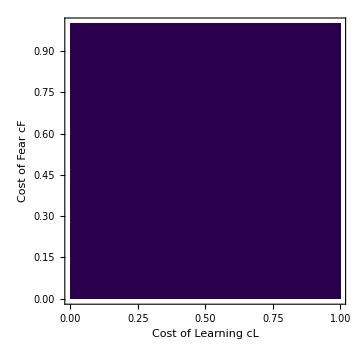

```mathematica
data=Flatten[<<"dataλ1",1];
costλ1plot=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,12],ImageSize->Medium,FrameLabel->{Text[Style["Cost of Learning cL",Black,20]],Text[Style["Cost of Fear cF",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### λ = 8

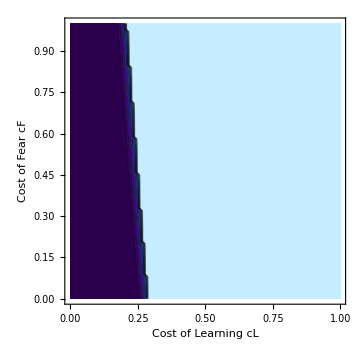

```mathematica
data=Flatten[<<"dataλ8",1];
costλ8plot=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,12],ImageSize->Medium,FrameLabel->{Text[Style["Cost of Learning cL",Black,20]],Text[Style["Cost of Fear cF",Black,20]]},ColorFunction->("DeepSeaColors")]
```

#### λ = 15

```mathematica
data=Flatten[<<"dataλ15",1];
costλ15plot=ListContourPlot[data,Contours->Table[c,{c,0.1,0.9,0.1}],Frame->{{True,True},{True,True}},FrameStyle->Directive[Thick,Black,12],ImageSize->Medium,FrameLabel->{Text[Style["Cost of Learning cL",Black,20]],Text[Style["Cost of Fear cF",Black,20]]},ColorFunction->("DeepSeaColors")]
```

-Graphics-

#### Grid

```mathematica
costsgrid=Grid[{{Text[Style["λ = 1",30,TextAlignment->Center]],Text[Style["λ = 8",30,TextAlignment->Center]],Text[Style["λ = 15",30,TextAlignment->Center]]},{costλ1plot,costλ8plot,costλ15plot}}]
```

λ = 1 | λ = 8 | λ = 15
-Graphics- | -Graphics- | -Graphics-